```mathematica
(* Look at stable distribution and infer what best payoff cap is based on underlying distr params *)
```

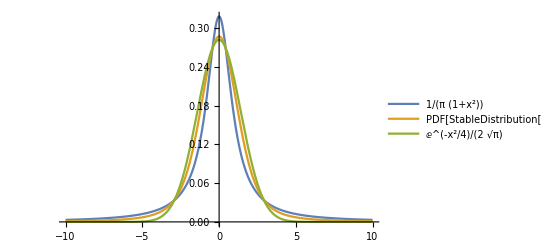

```mathematica
Plot[Table[PDF[StableDistribution[1,a,0,0,1],x],{a,{1.0, 1.5, 2.0}}]//Evaluate,{x,-10,10}, PlotLegends->"Expressions"]
```

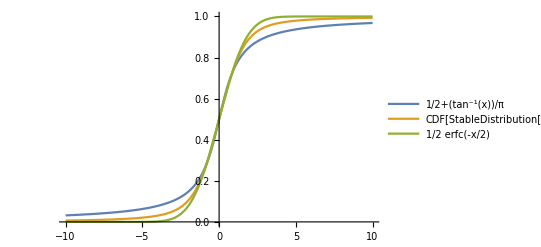

```mathematica
Plot[Table[CDF[StableDistribution[1,a,0,0,1],x],{a,{1.0, 1.5, 2.0}}]//Evaluate,{x,-10,10}, PlotLegends->"Expressions"]
```

```mathematica
(* For alpha of 0.05, can essentially put cap on x as CDF(1-alpha). Which ultimately relates payoff cap to VaR metric *)
```

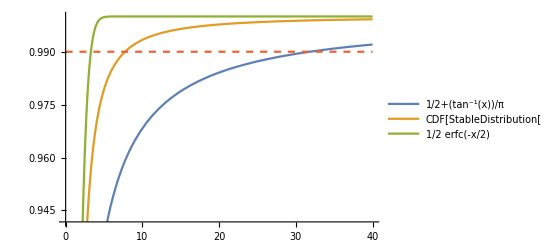

```mathematica
Show[Plot[{Table[CDF[StableDistribution[1,a,0,0,1],x],{a,{1.0, 1.5, 2.0}}]//Evaluate},{x,0,40},GridLines->{{},{}}, PlotLegends->"Expressions"], Plot[{ , , , 0.99},{x,0,40}, PlotStyle->Dashed]]
```

```mathematica
InverseCDF[StableDistribution[1,2,0,0,1],0.99]
```

3.28995

```mathematica
InverseCDF[StableDistribution[1,1,0,0,1],0.99]
```

31.8205

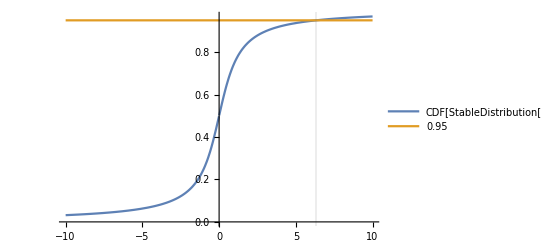

```mathematica
Plot[{CDF[StableDistribution[1,1.0,0,0,1],x], 0.95},{x,-10,10},GridLines->{{6.313751514675042},{}}, PlotLegends->"Expressions"]
```

```mathematica
Solve[CDF[StableDistribution[1,1.0,0,0,1], x] == 0.95, x]
```

{{x→6.31375}}

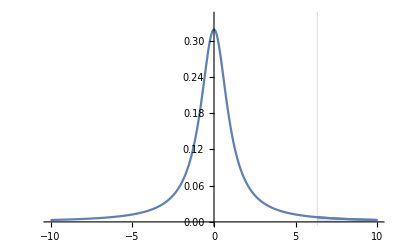

```mathematica
Show[Plot[{PDF[StableDistribution[1,1.0,0,0,1],x]},{x,-10,10},GridLines->{{6.313751514675042},{}}, PlotLegends->"Expressions", PlotRange -> {0, 0.34}], Plot[{PDF[StableDistribution[1,1.0,0,0,1],x]},{x,6.313751514675042,10}, PlotRange -> {0, 0.34}, Filling->Axis]]
```

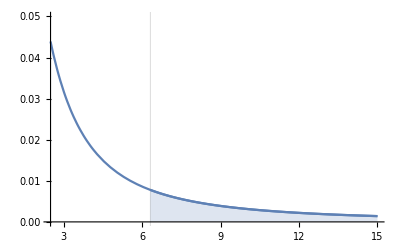

```mathematica
Show[Plot[{PDF[StableDistribution[1,1.0,0,0,1],x]},{x,2.5,15},GridLines->{{6.313751514675042},{}}, PlotLegends->"Expressions", PlotRange -> {0,0.05}], Plot[{PDF[StableDistribution[1,1.0,0,0,1],x]},{x,6.313751514675042,15}, PlotRange -> {0,0.05}, Filling -> Axis]]
```

```mathematica
(* Payoff to a shorter for a bearish OVL trade on inverse market: PnL = N * P(0) * [1/P(t) - 1/P(0)]; where P is # ETH / # OVL *)
```

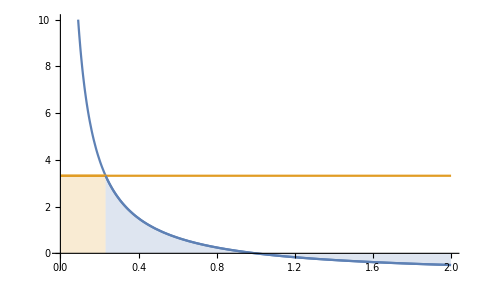

```mathematica
Show[Plot[{1/x - 1, Exp[1.2]},{x,0,2}, PlotRange -> {10,-2.5}], Plot[{, Exp[1.2]},{x,0,1/(Exp[1.2] + 1)}, Filling->Axis], Plot[{1/x - 1},{x,1/(Exp[1.2] + 1),2}, Filling->Axis]]
```

```mathematica
1/(Exp[1.2] + 1)
```

0.231475

```mathematica
Exp[1.2]
```

3.32012

```mathematica
Show[%86,AxesLabel->{HoldForm[P],HoldForm[PnL]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%86,AxesLabel→{P,PnL},PlotLabel→None,LabelStyle→{GrayLevel[0]}]

```mathematica
Exp[1.2]
```

3.32012

```mathematica
1/(Exp[1.2] + 1)
```

0.231475

```mathematica
(* TODO: Get some actual numbers for e^X Levy process from fitting. smaller uncertainty level alpha used, means greater confidence in X max, and larger payoff cap to cut off tails with. This we might need considering vol factors from norm fitting were on order of 1e-7. Exp[1e-7 * 6.313751514675042 * 144 * 7] = 1.00063663 is a very small 7d payoff cap of about 100% on position. Likely want payoff cap of around 10x over span of 7 days, which gives Log[10] of 2.30259 max in exponent. Then know that 10x * OI imb cap is max amount we can print for one cycle, then we adjust cap down accordingly depending on prior printing on rolling 7d basis or something to strictly meet inflation goals *)
```

```mathematica
Exp[10^(-7) * 6.313751514675042 * 144*7]
```

1.00064

```mathematica
Log[10]
```

Log[10]

```mathematica
N[Log[10]]
```

2.30259

```mathematica
(* Inverse market payoff *)
```

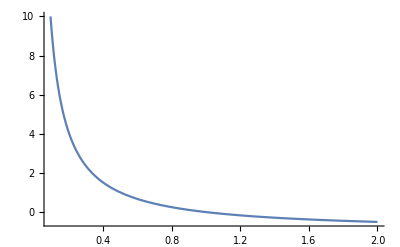

```mathematica
Plot[{1/x - 1},{x,0,2},GridLines->{{},{}}, PlotLegends->"Expressions", PlotRange -> {10,-2.5}]
```

```mathematica
Show[%87,AxesLabel->{HoldForm[P],HoldForm[PnL]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%87,AxesLabel→{P,PnL},PlotLabel→None,LabelStyle→{GrayLevel[0]}]

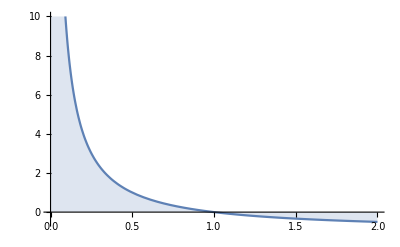

```mathematica
Plot[{1/x - 1},{x,0,2},GridLines->{{},{}}, PlotLegends->"Expressions", PlotRange -> {10,-2.5}, Filling->Axis]
```

```mathematica
Show[%93,AxesLabel->{HoldForm[P],HoldForm[PnL]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%93,AxesLabel→{P,PnL},PlotLabel→None,LabelStyle→{GrayLevel[0]}]

```mathematica
(* Look at how PDF, CDF evolve over time with e**(μ*t + σ*L_t) Levy stable increments *)
```

```mathematica
Manipulate[Plot[Table[PDF[StableDistribution[1,a,0,0,(u/a)^(1/a)],x],{a,{1.0, 1.5, 2.0}}]//Evaluate,{x,-10,10}, PlotRange -> {0, 0.4}, PlotLegends->"Expressions"], {u, 1, 10}]
```

```mathematica
Manipulate[Plot[Table[CDF[StableDistribution[1,a,0,0,(u/a)^(1/a)],x],{a,{1.0, 1.5, 2.0}}]//Evaluate,{x,-10,10}, PlotRange -> {0, 1}, PlotLegends->"Expressions"], {u, 1, 10}]
```

```mathematica
1/Sqrt[2*Pi]
```

1/(√(2 π))

```mathematica
N[1/(√(2 π))]
```

0.398942

```mathematica
(* Fits to log stable below. Starting with 30d worth of data .... *)
```

```mathematica
(* Import from csv *)
```

```mathematica
Directory[]
```

/Users/personal

```mathematica
Module[{directory=SystemDialogInput["Directory"]},If[directory=!=$Canceled,SetDirectory[directory]]]
```

/Users/personal/Desktop/note7/points

```mathematica
tblWethDai = Import["30/data-1624665179_weth-dai-twap.csv"]
```

{{,timestamp,twap},{0,1.62208×10^9,2823283256860140896256},{1,1.62208×10^9,2807416500389253480448},{2,1.62208×10^9,2795741643020610568192},{3,1.62208×10^9,2778509477732340465664},{4,1.62208×10^9,2767564848768069140480},3738,{3743,1.62466×10^9,1840325819329555202048},{3744,1.62466×10^9,1832467229514366976000},{3745,1.62466×10^9,1825074114325430403072},{3746,1.62466×10^9,1817085838281425027072},{3747,1.62466×10^9,1810494773684469760000},{3748,1.62466×10^9,1810804556505733136384}}
 |  |  |  |

```mathematica
Length[tblWethDai]
```

3750

```mathematica
FromUnixTime[tblWethDai[[2]][[2]]]
```

Wed 26 May 2021 21:04:33GMT-4.

```mathematica
FromUnixTime[tblWethDai[[Length[tblWethDai]]][[2]]]
```

Fri 25 Jun 2021 19:49:11GMT-4.

```mathematica
tblWethDai[[2]]
```

{0,1.62208×10^9,2823283256860140896256}

```mathematica
tblWethDai[[2]][[2]]
```

1.62208×10^9

```mathematica
timesWethDai = Table[tblWethDai[[i]][[2]], {i, 2, Length[tblWethDai]}]
```

{1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62245×10^9,1.62245×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9}

```mathematica
twapsWethDai = Table[tblWethDai[[i]][[3]], {i, 2, Length[tblWethDai]}]
```

{2823283256860140896256,2807416500389253480448,2795741643020610568192,2778509477732340465664,2767564848768069140480,2745828354088193490944,2727736176961791197184,2723904417120340934656,2704041208582260129792,2708998176205846872064,2708957922445429833728,2707680174482197053440,2695944365447723876352,2698373607653926502400,2680266501388141330432,2673423211281161650176,2666463989650712166400,2668925655655276085248,2672304892498461327360,2672264892061090054144,2671290004550853853184,2676102749609320251392,2680973189376187039744,2681086512517085134848,2681496690461062987776,2684094842685771218944,2685445606165706702848,2691518278792935636992,2699480089196197052416,2708909234860988563456,2714017949890912452608,2723546549897066446848,2728078648189622681600,2732798404365623230464,2736205750350773747712,2738549164965292933120,2740408402492291809280,2739886973103981461504,2738068641775508520960,2732878279417753239552,2733355381023297241088,2735655334127838691328,2741228286855930707968,2745848754848815644672,2757789870614201761792,2762280882964944912384,2770548567386833813504,2779513401456473931776,2783505730499585245184,2787899497467968749568,2790789899692304498688,2791366744634267533312,2790821263474369757184,2790556018381197148160,2790723452908507496448,2790770215307542790144,2791987724722161319936,2794184780804205314048,2799389501740996886528,2806764684938647699456,2814906782405361664000,2817371887757828292608,2816793185512886632448,2815366164781820542976,2809467116446830559232,2803470728561516085248,2801977345391733506048,2807923845137556307968,2816680080810950787072,2826351345374143184896,2829230819690937319424,2844881108177347674112,2845526938817979219968,2846056004686242643968,2847537689695054462976,2850418206824573960192,2851198229594175963136,2846520213412607164416,2835347528921623035904,2825295899203810099200,2818306064597918416896,2810326163623777402880,2802070737570245902336,2799446644260921147392,2792347962078446747648,2784202986476482330624,2778894244584430239744,2776590124688538075136,2776063976221398007808,2774667734541455065088,2775545755363831709696,2777110666599693549568,2781645777707600445440,2782809883603595427840,2783597626896385310720,2783565619960353914880,2783616107572831453184,2782461397921646510080,2780847045569229619200,2778801122423983833088,2770690494359044358144,2763685248750425473024,2758349054928008249344,2751085303850299555840,2747635811933147365376,2746684526882016198656,2745777520215356080128,2741657219691517050880,2736040761441577861120,2730118456546317303808,2729194017367816404992,2732073404375411195904,2741814525208712183808,2754154590660082008064,2764600990201965182976,2771245643847911342080,2773747676599470784512,2773168989326951841792,2769723084663710285824,2767468909441710030848,2763474904951046012928,2754264607258120290304,2748689397428054392832,2747284647969646706688,2738768647034475905024,2737106038072822726656,2739042347835879063552,2737714545797494734848,2733199537401500270592,2727639776629335523328,2717504941397481881600,2705675741654665920512,2701537295952182771712,2697386693391145238528,2697833286035274989568,2702383409000679473152,2707925931600913629184,2711426836160066355200,2713939904832290160640,2717579224720621436928,2719523723107732291584,2719435624658441338880,2718772745880854331392,2717163327721008267264,2716716369920546308096,2713364872708867751936,2709093145137512972288,2704647051181212303360,2697702822871428497408,2687881069334521446400,2676254047251147522048,2668674387213850509312,2664841002990548549632,2661195127090204114944,2650837013261041270784,2636595156561490345984,2615922641776669622272,2594696982634963140608,2567401983976658698240,2554259939355930918912,2551452139358452187136,2544467547703244488704,2545674672299568005120,2552634655835315765248,2557364095492908122112,2557229231440502718464,2559261135056533979136,2561840674093749764096,2559455747088770924544,2558199312797410525184,2558234570959686729728,2556533722662629801984,2543908364674857435136,2525077729337763430400,2504085048701372858368,2490954607443703758848,2471019747624511602688,2473771551094868017152,2474205166847904972800,2481032975362977431552,2488519306973876846592,2492668158123786108928,2494217096224088522752,2497473160151335174144,2498700692681369059328,2496066495681120436224,2490647212750100496384,2480260423432623095808,2468266186043695300608,2464500857293495074816,2470620023525346377728,2487411240705092747264,2503925670203742486528,2533392288718655062016,2554130874169823854592,2566444149740772786176,2574862228426089562112,2582260545870247231488,2592882335138798108672,2589981365543947993088,2586541825629257465856,2580291249896334295040,2573165344251791278080,2564902755714955476992,2558623747259639529472,2519054105422384857088,2553437164742240632832,2553979638739994935296,2555590762809308741632,2557106974284978847744,2595501137458207129600,2549471457340789096448,2539441349495296098304,2527537236155754872832,2519343115205811896320,2504826876758170009600,2500222370939434696704,2497075382716709470208,2494745238383013396480,2491598542381085360128,2495483668252450619392,2495043884592296099840,2492649337524945682432,2600896358324474216448,2496021223463499857920,2502102129387371495424,2508308939175044317184,2517939151397641519104,2413592805809920671744,2519753151904606584832,2512242187905643053056,2505552689556493434880,2501227521480031993856,2499615875874678112256,2494927399103606816768,2485555547005367877632,2469847087498739056640,2448364955761812439040,2421359451529212854272,2396680479223380443136,2378993805613700481024,2367329145684726644736,2363443991403113218048,2366141807959089872896,2370934520687806119936,2374631411817024847872,2377755789930748968960,2378498121596980953088,2383631682552525225984,2389372727675175567360,2396914492739486744576,2405896014948039393280,2408807316656603791360,2419859296068828135424,2427903557470575394816,2434682181423286714368,2444230879166102765568,2460019185309773725696,2474184057239067688960,2489237812431203336192,2505180746918871957504,2515657642287079882752,2519018250493201743872,2520767422394483081216,2518190148023447191552,2514784667239870627840,2511954597927563296768,2509849272772669734912,2507480066680908414976,2507491349842502352896,2511848413215039946752,2515511699456128974848,2517944192531270467584,2519854977656697651200,2522367676595569164288,2519141447245468008448,2517510088221603135488,2516258036432883941376,2508456761927634255872,2500795860112240017408,2498440363433322872832,2511110178609707352064,2519857617219772481536,2532161703416493506560,2546987349195713675264,2556730605436576202752,2548204077968568877056,2546001124171610849280,2720404121477766447104,2540969987798688858112,2536402576658041143296,2531401878522376486912,2523108235309858422784,2322151657675870961664,2505792289942667788288,2496802532447629606912,2486728414798425358336,2481273357378150465536,2473657263267289497600,2466883898337083260928,2457772413614219067392,2446156390761049358336,2436336018925058260992,2428782132438112927744,2422255885024042680320,2422970639702658908160,2423725761651696730112,2426027551577464635392,2427313529624030347264,2427153316335251357696,2425636091167732400128,2423738039430212485120,2417609013878362996736,2420941218413676593152,2424258965240024662016,2428462021358738472960,2431491786797317881856,2439317568990628806656,2432728170292760281088,2425803422289357701120,2415400270012133933056,2408724593632735657984,2399525844886725591040,2388327531183771484160,2377372286317691404288,2370966492930961309696,2368958922356735082496,2378698763975640219648,2381261074101446901760,2383249763378020220928,2383349706933223817216,2381019069348638621696,2363721355825041113088,2349789120172185092096,2339036833022407344128,2330463437375719866368,2322139130728585363456,2316740207931736195072,2317695470187027365888,2320361306119120355328,2326580013440134807552,2336575633208275632128,2343571846044937879552,2345523491187067453440,2341412724437374992384,2328160867641592119296,2309940886570856873984,2292328948411657093120,2282051905432268046336,2268576893172937129984,2263343994718073651200,2262342945994831036416,2263337602828059017216,2264095801623798611968,2258173178879050252288,2252289157505998913536,2250241095917905641472,2248876442371697410048,2244236203581888266240,2242641905315534077952,2239773327464722595840,2233875521155791323136,2228836968636968337408,2232843070785021542400,2236648104912550363136,2237195445281073659904,2242680699555422142464,2248375923489227145216,2253356111269609340928,2257170431802223362048,2263784536606981488640,2268203867222083371008,2267596022037898854400,2265185175745727561728,2264805976942186070016,2267152951782084968448,2274185225482086121472,2280251556297338519552,2284257626830097350656,2285346105234963562496,2275902345532490907648,2258592434298569621504,2240259112253659545600,2224292279123258114048,2219125214757827379200,2214347698319897133056,2212919511201861074944,2214898705862768197632,2214980837063881129984,2212108389112826560512,2214239285407443845120,2219038517169432821760,2228195558270298488832,2239727314472643592192,2244889727562655989760,2259377460932225007616,2268323771509710782464,2276698677571690954752,2280434220083787857920,2280272596302164918272,2284672533539892232192,2286504837294655275008,2283640700188101181440,2284179565280738148352,2290536927134924144640,2292510256086412951552,2294068699445464924160,2301792303038777786368,2313127375851468095488,2322762095805745070080,2332066459418882473984,2348825811203421372416,2362773749040786964480,2375171995237565857792,2383735264508229189632,2389818086855935000576,2399003279267403923456,2406177659181134249984,2413088879769351094272,2418079187044910235648,2422923331640665571328,2428738583183230500864,2433068033040819683328,2436728357096947974144,2440639857249803042816,2442162048306789744640,2439497726913257406464,2436009395958482206720,2430850531980424511488,2428736046156604768256,2428539312246860808192,2428218667876490936320,2426285827203496148992,2424443119422261428224,2422634124671429640192,2421280772446745526272,2414685641922122350592,2413167864256971931648,2412098244603127791616,2410435911485065003008,2407964497416675131392,2409837353878649044992,2409089040030579556352,2406936341500033761280,2409990821034354802688,2416132174290223104000,2422463985835006492672,2426991936485537087488,2432516611941791170560,2428794284465060839424,2417097738362019643392,2404569023823657041920,2398917033407909724160,2392241724329568501760,2386698034199302504448,2386820975277023690752,2387321713440575193088,2385944404977285857280,2379408682027560992768,2372882240904831172608,2367258961065145270272,2362003591674879541248,2356871657073051172864,2356902446378294444032,2358451988811813748736,2359751911227686912000,2364007131836758097920,2368629330499039395840,2378065985509337858048,2390069350483627081728,2394722955101015638016,2401283795339037376512,2408459189628832317440,2411212904729735069696,2415056174014640160768,2417282066002721898496,2424458019038051172352,2428680339574115794944,2432196489134873247744,2436640247938106261504,2438850838827532025856,2446882552339466551296,2449959474720159563776,2450494754347279712256,2450690925929443098624,2449801621951049891840,2445360028262869237760,2441147454230376218624,2441398318899056345088,2441231793595948204032,2440483295563760533504,2440167222825230270464,2439742512861683908608,2434754585667057483776,2433526861806888812544,2432795708960204128256,2430564051215398207488,2428807382522874298368,2427196119823171977216,2422380466158122303488,2416183727128206901248,2413578561024218890240,2408699726227083624448,2403182170350860369920,2399908210545170317312,2396299498033665540096,2391469454117438488576,2387504255763645202432,2388532284102656655360,2385243742941454794752,2379443343517507649536,2374763208559244083200,2369620299216871489536,2362279360648227848192,2353292979922624839680,2345652560294698024960,2338482034639488679936,2329663334532047962112,2314232317492114489344,2310405710275992092672,2304603683678934007808,2302292146883544219648,2302579390120498823168,2305939123461628362752,2304988695182578810880,2304124486463766921216,2305147576852175126528,2303564170143304515584,2298483171365887410176,2299830086245623005184,2302327491702240313344,2299944593724148023296,2298865791116272205824,2299391258943584468992,2301733990431579176960,2301621178760467578880,2304306096636824911872,2310603934131796574208,2315559879755051827200,2319696790210039250944,2322788009533644996608,2330389634791029604352,2336501601687432331264,2345440323437380239360,2356976345899373428736,2365513621003247812608,2384707209845156610048,2395965941133844938752,2570155672313468551168,2574426340567860379648,2577297958474596483072,2580598572048631463936,2582923918759191117824,2715565447663336816640,2708320856724176633856,2697616133879103488000,2689638458975778766848,2675878430432149110784,2661244361886489116672,2651259983865066815488,2643990812401452711936,2636278099382840590336,2632083320878064467968,2635492743812619436032,2644207014314722721792,2643764831864321212416,2642904445222627835904,2641258453581325926400,2637012014478445248512,2628603021920060309504,2630558503477801648128,2635896114941285367808,2638525968591772188672,2644120824206141685760,2650567972795703099392,2659916487470537506816,2673114179195965014016,2683956717182165975040,2685933267297769619456,2685080060275754270720,2675062207335093501952,2663971586427732361216,2658670363307478089728,2654528051287994925056,2651833352640819363840,2649403121723301691392,2647761752567619518464,2643340139191984455680,2635311084036790681600,2624868757499244707840,2608494199904827080704,2594056292821190049792,2580016635481439600640,2576547618060458524672,2573751713689808404480,2572038794078543413248,2571690105143018651648,2570803840380943466496,2569585899440709304320,2572058490002816368640,2576547261802220093440,2583835977827362013184,2589984876089064816640,2596372934966450323456,2599300208001102643200,2604470050976481411072,2608965583553158971392,2614262308079360540672,2613683375790018789376,2607980477262178811904,2600001163007632605184,2594122755658051223552,2582242436930206695424,2573411782055848050688,2563741010803231817728,2561703180254293524480,2568258804597876850688,2577856271758306836480,2590063351562627973120,2614022428669226516480,2621945707621852381184,2621132670648063623168,2617020992052972748800,2610920347688779120640,2597623811078779043840,2588724381491402899456,2580652861936397451264,2569860419151654813696,2565061742170170982400,2562791380974667038720,2561105273158941802496,2560904197825929150464,2562568583776719863808,2560399743385491996672,2556142720892846211072,2552134783221719105536,2546271821713339056128,2540647440465291378688,2540423140733955866624,2542942782666516201472,2545945014178631122944,2551816519083655954432,2555716954514953076736,2560249974827626004480,2563251352072093696000,2563447932406450356224,2562524654913445167104,2560608184885893398528,2554257703375054307328,2548240327584565428224,2546405738505652142080,2543900644491517231104,2544843799964662890496,2549632112590009663488,2555072110007625973760,2559993476334450900992,2562762467649068728320,2567383026853496225792,2570104632170916610048,2570960340486723731456,2573775570396795895808,2580955334073237635072,2585624186840585601024,2587618182047589203968,2589565272619846467584,2589152040359995899904,2587790032932859543552,2585821084075665915904,2589105416686426128384,2596543982076617031680,2606254834893351026688,2613863200457767256064,2621283258933720907776,2618328609127445561344,2615255135840546848768,2611636447366026362880,2604168221139739344896,2594361413082867564544,2584993953804480675840,2575955864390780583936,2567652790401450377216,2564552401229082787840,2568448436077789184000,2574682604010515464192,2579605434526716133376,2587855810292561739776,2596487626709738192896,2600408793297687937024,2604063351643506212864,2609021001067092508672,2612930114119166066688,2616351596450805710848,2619191587591824605184,2619223320230168625152,2619156156582687932416,2620083646834565185536,2623237009308826206208,2625312007349457649664,2625611378829620150272,2624537914431297290240,2622157765459527598080,2618914195134614077440,2618394709803829559296,2619179471029016723456,2623228233724758851584,2627226958497937096704,2632371798373776752640,2637631444229387976704,2638831870692116922368,2637965209252937072640,2639960019335621115904,2643024145488400613376,2648965445164438388736,2658856923693062291456,2671772414101494431744,2679241928585557049344,2683791894013387735040,2688090079455627182080,2686992149721250791424,2686532291564848283648,2688314968920696553472,2692520396635379859456,2694707288270545879040,2696555940261351915520,2697613106743785029632,2696418604116663074816,2692964266891175002112,2690836394469534203904,2689173164908408209408,2687554488869799329792,2685586653425402118144,2683545162951967113216,2682989960692622163968,2680307485490012487680,2679372465322754834432,2679463691638466936832,2683327949371106394112,2686364551382130753536,2693080043099917910016,2698331561377800388608,2702635599349491433472,2704180526201060196352,2704100833018444775424,2700933199924669448192,2699251230540603326464,2703857240344843255808,2709868450666276454400,2716404237381523210240,2724403777165872594944,2730593507311706177536,2732121709245693427712,2734382606453125414912,2743316838597805473792,2750925315135166218240,2762328823190813409280,2773039763521783463936,2774717755595034722304,2779074220044939952128,2781289429840635625472,2782835037189942280192,2782217373987443310592,2782999304047485779968,2780398292066226405376,2775747016539446444032,2771429144432819044352,2766941230452612005888,2761780422068625997824,2758514208699430469632,2758013814773513715712,2757473046634811097088,2758024973535523897344,2758670589537276657664,2760572664829948985344,2762352110308484448256,2762949051230390321152,2763754137442586722304,2764324748310359310336,2765096950380719243264,2764476272107675189248,2763224462695417774080,2761803141367356981248,2759773479385558941696,2752755996184318312448,2746937792643180003328,2740793266107054555136,2734617831012473765888,2729234559713018904576,2727151595445431042048,2726520197139707985920,2725209570702397014016,2724889792943674097664,2724660023915124359168,2723732963558363758592,2721093155408199024640,2714212798297926533120,2707385374207747555328,2701124504532256030720,2696179532642198224896,2692597612352530022400,2695869970057652076544,2702116521682063065088,2705765933532933783552,2709267648916128006144,2706833037667003269120,2704471433963292852224,2701673426482421039104,2699143997241957548032,2697384857530353582080,2699797896454806175744,2700735320334001504256,2700275001247265718272,2697939085685949464576,2692952766757443469312,2686846355784343224320,2683274793619035258880,2679115599084985516032,2678335774984018853888,2684812661346314747904,2689044452270794080256,2696100835295861145600,2702291940650498654208,2709241091567094595584,2719874817218445312000,2725783873484140052480,2738473416198420168704,2746288987486025678848,2754234151564481134592,2765982989701810749440,2775404424115273072640,2784575938540402638848,2793798409572372709376,2797038221217986772992,2802613103337400696832,2807410250819032842240,2815084253981420027904,2821649526109739941888,2824890369953852555264,2829403940225479081984,2828528355306029187072,2825114169512691236864,2819191200419916283904,2818106611924882423808,2820080758008356274176,2824303371074664398848,2827426427759331115008,2831566641311877431296,2834271543358982193152,2837376414485655322624,2841241683656176566272,2844179489416269004800,2849373021065796124672,2856015830866606424064,2861268159146455728128,2868542930345550413824,2873664353163396775936,2878269371792918839296,2877900038235768225792,2870889122125730807808,2861715674020881367040,2852354485729265451008,2841850968198912409600,2829471967032912117760,2817788309550676312064,2809539140701844406272,2806224975751649689600,2800352080504099438592,2807828202021187485696,2815800725680400367616,2822993854803646873600,2820675616902295322624,2816010872211967574016,2806513206311457914880,2796955821806475280384,2790085281828187406336,2782565822307406708736,2779596123155906691072,2779987520962858844160,2780582100211340935168,2782202029952323813376,2786642510601519628288,2790276006446543405056,2794284413780576698368,2794819358669391003648,2792744412461941653504,2790008625698914697216,2790747815788384092160,2793576588354534244352,2799513057666381381632,2805467344923761049600,2814778378464306659328,2822283305580246859776,2827088354152751300608,2829462169267187744768,2829824804995829071872,2830133780667060191232,2830760056737062977536,2828656833920909705216,2822334938624491520000,2818588591918992064512,2811625346913289633792,2804918406377644228608,2798226329042042748928,2793694189314385117184,2792466350992074997760,2791647752059193655296,2791490267644879699968,2792462598748105080832,2793266127143517028352,2794431737058507096064,2794927283455135842304,2797328681960259190784,2803050952204222988288,2808946285848189992960,2816656477979203338240,2819545988447223152640,2823729886160320200704,2822576419421482909696,2821259741365709832192,2820615153010139987968,2823804013550949105664,2826824817411424256000,2830077430587885355008,2832849080820258308096,2836516060133680218112,2845046041733353177088,2849645424714348756992,2850883365434955923456,2847627880480539410432,2841872421412359634944,2830062423041989672960,2819996696953785679872,2810312396830017060864,2798119564928268369920,2784310828522269573120,2769988719236831248384,2758591769768837513216,2737262207437555367936,2726384793619426443264,2721447497966703607808,2717499308780138004480,2714918174819131850752,2714431254502593527808,2720120309083598749696,2726364775644996829184,2731961272919092887552,2739218376251850358784,2743120416675640377344,2751373727214955134976,2752928365405542547456,2750239997766776389632,2745792420734033199104,2742144449980316778496,2732818092727986552832,2723235547191651074048,2713971641941634318336,2698457566491047362560,2685542003995193114624,2672406956888630493184,2666190902748739272704,2662393088543472222208,2658414295364322459648,2651130686284943589376,2640057772229162696704,2627654379032925437952,2617246381883468546048,2610825312568304730112,2611948726409550626816,2613484614123104763904,2615618176938780131328,2619508040157724409856,2621862747874543009792,2622297698169066094592,2625108778696560345088,2624027862454389178368,2624100395050634051584,2623180441734873612288,2624006751375628697600,2628004046914858254336,2636820241750474883072,2644249605412866752512,2648948571941968543744,2648685102609653563392,2648655527752942223360,2642773235354306084864,2638406771050904813568,2636429784113519001600,2634956538187663015936,2632315566968007032832,2630931529244186509312,2618715285062291554304,2608073138812456271872,2599089328882822152192,2593067839944002633728,2597308929097398747136,2608852971672587730944,2622525710093482721280,2639534541706350297088,2645508657392803381248,2647946803644063547392,2648775297179021475840,2647652318556022898688,2640877961650851807232,2637720263456633389056,2631990390261202550784,2631030207959252074496,2633179387986335760384,2638148422514275516416,2641445316995047751680,2644980232469751005184,2646769897685868609536,2648739671947223760896,2654804054872351047680,2659605625232196894720,2664184637349025546240,2667850311140343021568,2669131910379433623552,2667173657201115398144,2667039761401466847232,2672347297817941245952,2679974222071630135296,2688030022035024379904,2693758389024537444352,2696153720775629078528,2694792833888695091200,2692338757786157449216,2690290897227198496768,2691451574454483156992,2694752877526071115776,2697385012802820243456,2697152303996270018560,2696592967115530043392,2695524238934196355072,2689874535454144987136,2687190583265633239040,2686142942803880050688,2687531526604793053184,2689060928474332528640,2693690162161369743360,2699350857103040839680,2705721505402915389440,2709063183236070375424,2718936884886513909760,2724281242538555736064,2726196054371892985856,2726196665823832571904,2725650845540048437248,2724027077477640175616,2723742797846887792640,2722717294896466624512,2719074210779900674048,2708111435538553110528,2699318569009382162432,2691136456519129759744,2683886049516130402304,2680837503199937560576,2688535102126789492736,2698345376632750997504,2707812329822851956736,2717888804620991987712,2734686794573074137088,2743059798661351866368,2752105502350137360384,2755797345400431050752,2757148921591678107648,2757880889731853582336,2758046883928524980224,2758853869037867237376,2759109303770352189440,2758712233692134113280,2757538017916176826368,2756782935961177161728,2758047383296636616704,2759994833160400535552,2761320147972558684160,2763213739451681341440,2764387160616504655872,2763816261876744978432,2763467732307190218752,2765514693172156432384,2766651637986621390848,2767561022681744146432,2769817199419974483968,2772214499764408418304,2773782633859547922432,2774755272310714793984,2772952772957045784576,2771117168277620523008,2767679606440676294656,2766706770430219780096,2766723770129794990080,2769241488533198733312,2771460285372795191296,2772668179819335778304,2773675547628049793024,2777198899141338988544,2781173246166026944512,2787919873151630573568,2791188780501537652736,2793619472016286416896,2791915671989643116544,2789737879040082575360,2789266044233454190592,2791544841467622064128,2794467353276905947136,2798285454632618557440,2800439776350452056064,2799874850304201588736,2788262726201440206848,2770370185548490866688,2748045109161638756352,2734342966433489616896,2717807240567132782592,2710383700657850810368,2709595216507008188416,2710826599718893649920,2705696349376126386176,2697920182238763810816,2688211554593118093312,2675393491568958111744,2658360523072982745088,2648066581317756125184,2642376442652575399936,2636613017906789744640,2637440536711394754560,2639050788381239803904,2636466995678228250624,2635839442919189643264,2634047940212958429184,2631072130773015855104,2628957943104132874240,2626163317410818949120,2623212741246948212736,2619807835267252355072,2617096920670101569536,2613847496168093777920,2611514165165617053696,2607758190372947755008,2605432371953832296448,2605269200310611476480,2613619098950207799296,2621958131420375285760,2629780661609822683136,2633732350429349019648,2636317008665792479232,2633532963611773763584,2629290244823484727296,2626090267372678021120,2624250842107195949056,2622418739006792007680,2622660138734963916800,2622564232392795488256,2622407220600031936512,2622694367017376940032,2623077544397755645952,2623492794702473199616,2624126240169202286592,2625189870661865570304,2625494799101880958976,2626363655232249397248,2626778667343339847680,2625541995874736930816,2622272537382309330944,2622233597006331248640,2620106881561145114624,2618729606513426956288,2620027072757396144128,2624112404092066725888,2623856292520083324928,2620317009088204505088,2610591612893098672128,2596880776513925414912,2583709130426719141888,2577722871185819041792,2567310345647206957056,2569468233822292672512,2572435217228513673216,2574892279715737370624,2575405095932781395968,2578174202102379708416,2580754406509080739840,2583121301858383036416,2588998502044324069376,2596151047977263693824,2603244954086065831936,2609948133392020668416,2617591258532937203712,2623383067156287062016,2625069888654662434816,2629994022251346264064,2636435943905350385664,2642803444718302658560,2652868266916373856256,2660413794848968540160,2666812281636131438592,2669942768531790102528,2674883313630384750592,2677909780179792166912,2678795297407415353344,2678192716519419936768,2676521363327955238912,2675040115862851289088,2673521923105510391808,2671658892462815444992,2670627503929776668672,2671875709776338878464,2672462478108009693184,2673736884058100596736,2675493568505359892480,2675939504481405763584,2677213463098821705728,2677986831165727178752,2678233060846608580608,2678303718147416915968,2678878537409630306304,2681833982027587125248,2683435051320436850688,2681513171639566598144,2676686714612343635968,2672921918549377155072,2667083237538741092352,2661719792652355371008,2661988284927158779904,2665549973287005061120,2669215500132935008256,2674118424782762409984,2681454677656785649664,2688733379286913253376,2696536271202404532224,2701592000713647456256,2707983771105833254912,2714089583509649752064,2716409119397917491200,2720553759460491264000,2723569866302833557504,2726333211622327713792,2725023669652498153472,2723333363224083431424,2720542359757736902656,2718225535742860328960,2713631987936247939072,2711533839101668622336,2709782564898963718144,2706880336126628331520,2704438807212788285440,2702617553445506252800,2699799901682844827648,2696212142411504156672,2698100252550853820416,2699371321017680003072,2699915228859516583936,2699915911640827035648,2699370058039511482368,2693788366008388943872,2687087661441708720128,2680920616219444248576,2677841395296954744832,2669794382253762019328,2666076540479315378176,2665898404841840443392,2666041919148028067840,2669388580037979537408,2678608684261605638144,2690774761233281187840,2698725897796276715520,2710453182245971689472,2715156279961744048128,2716919993829825183744,2718061483747350413312,2719215802103610998784,2720331402756750835712,2722128729586926616576,2723185160971300110336,2722113363733542600704,2719707557221259280384,2718243882330505084928,2712719187779361701888,2704295516426603069440,2700710689404225060864,2693876837540675715072,2692336528961136230400,2688478920398032863232,2687600506603253006336,2687144446380647907328,2686157458118444318720,2686195363314004918272,2685787914002045075456,2684404369708306399232,2682697124814457405440,2681740349001905471488,2678922985718959046656,2677986003615958433792,2678111773747611435008,2679906988766092328960,2683174983925048016896,2688556835436257869824,2693737429284208246784,2699620327316393033728,2703256157160689106944,2705335853491059949568,2705033498714073202688,2701407847938796290048,2696392093710641266688,2689769059653019238400,2685364357106039259136,2683948103064028708864,2686536092659138691072,2689427374118231080960,2693309663507626065920,2696244234897789026304,2697928679815854424064,2706737229682764677120,2714150319476261781504,2723004391884826083328,2732585657129100640256,2743140383608634605568,2746995323397418778624,2748781728920036704256,2751482994025877733376,2756259043327769837568,2761197309679982084096,2767482709501035937792,2775620288131434020864,2782442315195442266112,2785073303358075830272,2785207597365401747456,2785425919820821954560,2785823254882043822080,2785685705853010706432,2782647013692578201600,2778435278247358365696,2774070884315606024192,2772031866009912082432,2771882943166036836352,2772253211054183546880,2774280090814051778560,2776893351867510685696,2775424869160026374144,2774020486941357113344,2773653823167385829376,2773412962999320707072,2773183255588564369408,2774329317285708169216,2775266331216372563968,2777003418345335685120,2777950004460533579776,2777395892282270941184,2774261633968572989440,2769245593671445250048,2762180630697761308672,2756870986701298728960,2753477282569022078976,2751938600210181652480,2754482268930942959616,2757321468672492961792,2758725103783591280640,2757284011308290670592,2755854504271482454016,2754039895480906809344,2752224714790082183168,2754733344398484439040,2758332799846182813696,2763804017556298137600,2770837445431034118144,2779976201974185459712,2789193293235395493888,2801128341106827198464,2808679628154843168768,2818346104402279923712,2821672805533246029824,2822229710556706111488,2818494451480592384000,2817033411386196099072,2814999763365809094656,2813808985922332000256,2814499488245421178880,2817305690489527205888,2819767433382336659456,2824648723826162008064,2825608650780186247168,2822662257563326218240,2817948222995668402176,2812010998491862007808,2801384434971808104448,2792552931708039593984,2789134993692784328704,2783802406694165151744,2776629352676534517760,2774424819579513995264,2772985041575743062016,2773075345543245856768,2773157108425373515776,2775915994428248948736,2777450178286117715968,2777951545625145245696,2777242556486294437888,2774783644108062195712,2772738657112684494848,2769954320513141047296,2765265469758097063936,2759467341816643190784,2750580496726975578112,2745128987288049549312,2737476397314345533440,2728895612734500503552,2724631542662223626240,2716602583356122595328,2711320110770686001152,2707022289091279978496,2702182096248986664960,2695597723806906974208,2695315571684145102848,2694034209233158275072,2695343281551967256576,2699158801191407190016,2705425587724472025088,2711907263701455994880,2715876281149443538944,2716572926687182848000,2714821372057479544832,2705840964680116862976,2690823867451979595776,2672848837460775403520,2648482030685098344448,2626390525271912480768,2615417441378332835840,2603140897547919818752,2604098065338088816640,2607273971367855783936,2611078763289598492672,2613374253649909776384,2616171191241508651008,2616183625318517964800,2614837078319896199168,2611552913874109333504,2609087727684716331008,2603356837901687062528,2598164691713307181056,2594083590878683725824,2594559459831084220416,2589754041995642273792,2585972137830920486912,2583597551885271695360,2582885272097580384256,2580765949066344923136,2588143139542656876544,2593688367211491622912,2597898520074588782592,2599062275301398020096,2599203206646638575616,2596964323366239993856,2594589575602183864320,2580940843918548271104,2562651472569532678144,2537895599872625082368,2514931310156167774208,2492964040725498953728,2479819244693315649536,2477143930296823971840,2480110203360453328896,2488489496657328603136,2498570991723067473920,2504189872401904828416,2505698046124118507520,2506545589019784773632,2503118243937222393856,2500171115863549673472,2493750119805662789632,2487764710461009821696,2484812168538570620928,2483972163465304342528,2482517145493242904576,2484958538470870482944,2487812994433725497344,2487359084428139167744,2481521466277859164160,2478274735240447000576,2481038045892072439808,2486256636595084460032,2488984735388365488128,2499426888782963015680,2509439788361951739904,2517257645371946434560,2523134687654517407744,2528042168272334880768,2535724252469113913344,2538436778314013081600,2535353605696542212096,2527729783823437135872,2517340743066694713344,2508284986827684184064,2502957378059123032064,2501267635987277676544,2502862911140450009088,2501137143028872380416,2500627811384015978496,2498287925729474117632,2495009804932363059200,2491854285040702717952,2507551882221181206528,2496711008282012549120,2501761732134535954432,2508163675337690972160,2512475813948814262272,2502653781183760433152,2518537697478862438400,2518431735652223549440,2515460704940810829824,2509952568179081347072,2504156380553605021696,2497382642541847904256,2491350472196993581056,2485126474167229087744,2474903000681456074752,2459787770025621323776,2440000434198897229824,2425090294894755315712,2404682948289050968064,2389435487085250215936,2382304780415361089536,2371113870064370581504,2359286977933680312320,2349331685919209553920,2347573630483040567296,2348612326403148087296,2366628601682375737344,2382992524166543441920,2396301460342430498816,2402643543703078567936,2404808349354760339456,2403672631017622994944,2402605074733108035584,2401518825232539320320,2402255879382576922624,2403825134587114160128,2407131710994063556608,2414632174273932296192,2422201395074361720832,2433782724341738242048,2443876961684248592384,2453561422377404858368,2460351843317494317056,2465582073888661045248,2470778190016284196864,2475397574018373517312,2479018616298130636800,2482070399460519182336,2487430130832096886784,2493241935570598363136,2497524052013556432896,2507422984204870746112,2513436429239923507200,2520058147437240385536,2525852057666254274560,2526153720946853150720,2523687658321769660416,2521026678566013108224,2519187891182842675200,2519356269902538211328,2520918538207370412032,2528155368253980934144,2525219158280942125056,2524972487406426521600,2526102918036590166016,2525729472480836845568,2519896099479968284672,2521989152003403022336,2520800481268448362496,2515544630332974694400,2507533289843445989376,2501011666720457228288,2489156418627498409984,2479844234137880231936,2471432812804864212992,2466741992977146576896,2464743758922641309696,2462237054583590354944,2458316679268168368128,2454293836250361626624,2449459467162118782976,2442863090924668846080,2436055452147227557888,2435117952973741228032,2438575904260244897792,2441077433090166489088,2446950846136215142400,2453928935992780652544,2456264455685037096960,2457700424089014894592,2458478953543014809600,2451562990134263021568,2444280899096046206976,2438568806895024865280,2433597515457377599488,2434726148406491217920,2438124883911341244416,2451952781382999605248,2461782103482311901184,2471587102789929009152,2476819475278487093248,2478841813975702700032,2481037246009815597056,2486576430232524292096,2494839422131180666880,2504086698756340187136,2516879610035470598144,2524377979365657935872,2526064373364372799488,2526211801469576806400,2524369059834508083200,2517057925652035403776,2511786806294781886464,2506803788982437019648,2500356879616164495360,2494131034870982377472,2491825635335905214464,2488784276091795144704,2488632462319756509184,2488820946443345854464,2490904252366048985088,2492926520992246792192,2491059478359057104896,2488264885114041794560,2488872990729726066688,2489810105132828327936,2492539245827634233344,2497336353812403716096,2500469050759172849664,2501455805036506906624,2501389465311134613504,2506172241509608325120,2519250618880464257024,2530085595225515884544,2542019538942447583232,2553365122868209778688,2557159932978146050048,2552002759926867820544,2548652860568680005632,2541525251108566990848,2537614781544490074112,2533307629424631873536,2530230863321555271680,2531257311937571061760,2528227155730996658176,2526708848013300203520,2523996432796444262400,2517120233172678213632,2512567883774510497792,2513338576424460091392,2522849886810853605376,2532971263803778924544,2548533600473808633856,2560197310019780214784,2564331643884112707584,2568866731829282996224,2573627219701312520192,2582681373442609512448,2588989480751558295552,2594847189266609995776,2600460582749137797120,2601179285032332165120,2597854724472416763904,2596039954904954437632,2592445038315580162048,2590104412346973159424,2587721420712670920704,2585063641999337324544,2581024975233472266240,2575000405685274411008,2570014755127734829056,2567691649272217862144,2565600408023176577024,2563466548164533157888,2562623111473514151936,2561752317504707887104,2561106054265355894784,2561639432150576529408,2562311375527506608128,2563508989886828904448,2564165119843984998400,2566027787824634265600,2568359904054436429824,2571319406111576555520,2577106531049735192576,2585153278938502922240,2591423645836966363136,2595701583839957614592,2600467971739120828416,2600853678889147301888,2599458992777515761664,2598765655729103175680,2598495978204324954112,2599263773867781914624,2600581864762865352704,2599136024079593635840,2596899168411493335040,2592270070291717685248,2588113720728487985152,2584122241696169197568,2583229699540412006400,2584048326539055464448,2586597679788982272000,2588195862554280984576,2587199595675764391936,2584292265584540778496,2581125375847180533760,2576178290357398142976,2572772540004180688896,2569424663245117980672,2569586160058749681664,2570988713617032478720,2573662489263730589696,2576666289816529272832,2577839268983876878336,2577796635661764657152,2575266760705432354816,2571938377157203460096,2567361183107580428288,2562869740701000138752,2558470136057143754752,2555309868544112984064,2551976571509768978432,2546644970162775654400,2543263515479439310848,2540487811998966874112,2538398774927312814080,2534375130590288543744,2531897128879485091840,2531835217752022843392,2532314979970811166720,2532717856010587865088,2533374725957637111808,2536167186739328188416,2537425739310700167168,2538204495224619663360,2539458097697279967232,2540580484311103832064,2540449463980713312256,2539891325392318889984,2538858172911529230336,2535909903260545187840,2530543996766117167104,2525033392885231779840,2518385132028168765440,2512257688511253053440,2516343022877865410560,2522590893984695451648,2534970445740011683840,2548395363083930828800,2564306014270758322176,2576491308088262393856,2583222998425563824128,2586118065138723454976,2585060508090200227840,2583527342371664560128,2579285770250705436672,2575893288724792868864,2572879408443407466496,2570915224218427195392,2567375586594066006016,2562058097423104868352,2556257256231291322368,2552603655724900286464,2550544660764319809536,2548585565582845280256,2547324347902949064704,2546322986207005900800,2543528164334392836096,2540500759974209650688,2539141704848733372416,2535666596378872643584,2533932373454001012736,2530640019975246446592,2526180237191466713088,2521867687402146889728,2520476276065166163968,2520160841081225740288,2519314038242777497600,2517639619191840964608,2514729090899625639936,2510687714956361072640,2502909094865384505344,2495987664192045842432,2492200644938456104960,2487801599082437279744,2484914955178021486592,2480391888591578464256,2474737717046751526912,2469835487889845125120,2465579371907264282624,2462301699032960466944,2462548212679968817152,2464078008252241543168,2464527299545914671104,2464611544856754388992,2464369464271369666560,2464685582810004062208,2463137644183177134080,2460931674843728838656,2460895372250158989312,2461653738336520503296,2457899823808813989888,2454105869699861446656,2447734412035019505664,2442498065319141048320,2439457055778515451904,2440338384611831185408,2445437489475202056192,2453861247624948482048,2459627479137708408832,2462472708758009020416,2464853537829883478016,2469410921434184155136,2472863124072246018048,2475124343020938330112,2477791132979844612096,2480170070706810257408,2481497011751416233984,2481935456804848795648,2482443566482641649664,2483199108275620020224,2482463096152890802176,2477794244484260167680,2477891241985676673024,2474746413363066044416,2470979943602860326912,2465071318334104403968,2460913202092334120960,2450995101986218573824,2439558343307633360896,2433389609498277052416,2424231643103775686656,2420919159402910449664,2419898631893345632256,2418423646332954607616,2418311583359378128896,2419477736252144353280,2419348917729162166272,2422088576662671720448,2432196574945185628160,2440368301073036738560,2445862403295011667968,2450261906188835749888,2454185328068284383232,2455864258119684587520,2457343334805411987456,2459119356399121858560,2462120207864398610432,2466001271517989568512,2468291537339134509056,2471253676502551101440,2473724518360364351488,2473855164401173135360,2473298660222006460416,2471135422625784266752,2467013580942042202112,2462608491307802820608,2457439711192178229248,2451910593711621275648,2445418209515862491136,2439184975590561153024,2435100575080550760448,2431010631919956656128,2431950023393285767168,2431572931894137847808,2435446113711717613568,2440165729310042750976,2445094870909333274624,2448946808128090406912,2452068624463493595136,2453417273688028872704,2452672173805283049472,2452566173555602489344,2451425332608609812480,2455545885682257887232,2457945492051718569984,2460839680052621213696,2463673226468565975040,2464239699531162189824,2465077006465526398976,2468576344861920722944,2470355777938125225984,2470998531843573153792,2470747932189712187392,2469706304454430556160,2466876084208942448640,2464679312875734433792,2462683169455456911360,2460760234195309035520,2459319643936343457792,2457979397547437326336,2456901599691603968000,2456937673266424709120,2458333701240331960320,2460252834935822352384,2462406166251830771712,2464386691774717362176,2466590375058807980032,2466890685129769353216,2466608002402565488640,2464574259279600549888,2462400291125075640320,2458501279799700357120,2452248687404506415104,2445561639384626757632,2436788709468942630912,2429134863081352462336,2420963147570450268160,2416892131935139135488,2415372940176297820160,2411601406397187620864,2405652886770950340608,2396419400566471917568,2389664079900057796608,2381579373803857248256,2382379008547950690304,2385561930114712207360,2389391227031845339136,2394292000312850382848,2396011219269667782656,2395853149756660383744,2395158127131323531264,2394728251578342965248,2395771989860829102080,2397500082573699186688,2401858299841327661056,2404398329259763433472,2406030981809273569280,2406067656645995397120,2404043199587242475520,2400676188912438738944,2398227235937606696960,2397373617118177132544,2396431345902423638016,2393273820749502087168,2388754765267172065280,2382057106604471353344,2369349410712323620864,2356195902654176296960,2350240816316723757056,2344793970146449817600,2344145169850599735296,2350781728577335853056,2356748685670191988736,2361289001955971563520,2362233777248046940160,2357501047799315955712,2349831858028866961408,2345255080395606065152,2340759893727857082368,2339659297241125355520,2341072520086790602752,2342289378997884682240,2341647927621606440960,2339744955000885870592,2337672364894561763328,2336455724735118180352,2337305392552192770048,2332149329740027396096,2326046123284732313600,2318951364293038178304,2310307751708275245056,2297231270768012689408,2317956463755289952256,2282466455970572926976,2277273844783680061440,2273701227853411516416,2275347808466426134528,2251663575451959820288,2284843636842982014976,2286332330263843176448,2290147302710132867072,2291546396371875790848,2290725371462683197440,2291316309930098294784,2291789632675269836800,2289164455161532776448,2286773084781847511040,2284392714134367502336,2283792073613722517504,2284945050621253779456,2285999682658461024256,2286426937281973583872,2286759905435439595520,2286823867749924864000,2286994121331161694208,2257341702714195968000,2289155893736853733376,2294639013656889917440,2296350715016861188096,2302931843464126791680,2343196769077410398208,2313426907472913498112,2313623254736650371072,2313512363944791506944,2313410421468997877760,2313196284569950355456,2312424026418149326848,2311613150359340974080,2311912500477357719552,2312557484479174148096,2313176501116933242880,2314173262467605200896,2316251677487570354176,2318034365546434396160,2316782148458734682112,2325870650889875488768,2338881278814636474368,2352434668930192375808,2360557288651100520448,2377968891920638279680,2382094807344667951104,2381528277489661509632,2379949236908858015744,2380537895838419517440,2383752927227781578752,2390343820483261628416,2398610992079086026752,2411736868485627117568,2422499958241165836288,2427932186610769068032,2433242350818182561792,2433446297207424155648,2433462165560647745536,2433924911656216297472,2431711845485317193728,2428891048466810142720,2423596558073220562944,2420314587755146903552,2417909416383909724160,2418437465014646341632,2419084942127961473024,2419386098682145275904,2417758617323250909184,2413988784838109298688,2406357678624180011008,2403588149132068388864,2398350425236827537408,2393121433999287779328,2390885873340707241984,2388900338102816473088,2387383614391657168896,2386450591590869630976,2386417548019998654464,2387362972813576110080,2388471972081522704384,2391402512018200592384,2398051037499552169984,2402340884118531211264,2407292645677784367104,2410438373390285275136,2410581269398316122112,2410890066290029363200,2412256342158202634240,2413879348061301899264,2415310754294645915648,2416583523329481113600,2416409034046105452544,2415351924868165140480,2414051960290847752192,2413963182825184165888,2413700592288171294720,2412098373844796440576,2410850990745561595904,2409004083510134177792,2406767500389626937344,2404565685679954067456,2401126322979396911104,2401213128045708181504,2400490545315734618112,2397404876846757052416,2395354122791794769920,2390792187638147710976,2385068513765818368000,2381801207107517153280,2380791502428187394048,2381197020939730026496,2381534220503264788480,2381082328724075970560,2377545859144092221440,2373089851811965173760,2369247823062397616128,2364366140438267035648,2363999904021892038656,2370289455969571700736,2377680789821001826304,2385805411600817455104,2394835918266787954688,2401960748242684608512,2403702417185150861312,2404036414530201845760,2404367006111950700544,2403054440897997438976,2401433742239292981248,2399314404886903259136,2394399219958582083584,2388937009174793945088,2379053024874579099648,2367222605126403883008,2357806831272677343232,2346289789334329229312,2340631816502979854336,2335080393807048474624,2333980052342256959488,2334974470592226656256,2335517543475908968448,2336022822379791319040,2334695539507832553472,2332612571179090968576,2330101523875891773440,2328075000390912573440,2325039199234090074112,2323117761274663403520,2322340647511933059072,2321477795980985237504,2320303795535412461568,2320987167774208163840,2323727519154435522560,2326690365104277684224,2329063014288573333504,2331228043291198488576,2333291959748396843008,2332518887021910687744,2331155416192516882432,2329890514284160483328,2331503288924217540608,2335415478621047095296,2339610336510753374208,2345610524250355531776,2350308820151775789056,2352652665492917190656,2350860427203363471360,2349884331073117093888,2349842916141164134400,2351370654052622270464,2353152074477118685184,2357472924619646959616,2360210955640015421440,2363663231382906208256,2365346927534329561088,2366913732308424458240,2366693963901239296000,2366023006362868908032,2364774558619970568192,2363348229175468621824,2362887096610501689344,2363403233298013487104,2364567427783887159296,2365112417009014407168,2366117838625379450880,2364349409485700202496,2361304083308227330048,2358463648476928409600,2356047763571047661568,2354629657991153713152,2354410212857871597568,2355123896937749676032,2353873294749767303168,2350835873052783542272,2347384838717011132416,2343109010525972332544,2338903001243642494976,2336586963202514092032,2336551265252620369920,2336737753143310286848,2336928698294890659840,2338651929943704600576,2340076655942312656896,2345834842157864714240,2357458987318724788224,2368573585971598065664,2377214890177686142976,2388342382966828171264,2393436048238520041472,2394757909455827894272,2396088804457371926528,2398705255545287737344,2402867302821856804864,2408314082983007485952,2414284552587573198848,2418058228141873692672,2424911673547283759104,2428744453260266962944,2430342093713861771264,2430521301984563691520,2429325237378241003520,2428185106444677808128,2427608989971636027392,2427432762981596790784,2431941434237457006592,2440621916268867354624,2452563767603314556928,2464181026182759186432,2477542467403152097280,2493424810877675634688,2501245694828405587968,2509653596233692872704,2518166422013235691520,2523860847546841169920,2526043093155893477376,2525709533958372327424,2524583435940015898624,2520853450601798303744,2516494755904047546368,2514403584074046242816,2509119735754719756288,2506819288195183673344,2505214857547889508352,2503323557788593422336,2501208573479007289344,2502235306961253957632,2501417444335447703552,2500118572024402018304,2499116029640378417152,2498409322047434915840,2496053772688267673600,2495590487384796430336,2495340178129013440512,2496458688768483262464,2498953150669452738560,2500181822265970130944,2501446420213620277248,2503225512904505688064,2502639318363944255488,2500483935224350113792,2499801555144634007552,2498599143677347495936,2497572697675420663808,2496514774054734397440,2493426959991455088640,2489585333313964867584,2486170508492024053760,2481932309384369537024,2478254951710508711936,2477019061099436179456,2476959966875965456384,2476716085296822747136,2476449478148277927936,2477070210999762026496,2478096316457532522496,2480578504953053577216,2484797222494756929536,2488933147512751521792,2492974424888487444480,2495651751355681341440,2496205360632458379264,2495609041796329373696,2495140210479365357568,2494467787702533095424,2495930807781160386560,2496977787540321337344,2498326581252149215232,2498778477153763196928,2497777339782241189888,2495604205234195791872,2492272347783225671680,2487108775509728165888,2483432922995615072256,2480430598662357254144,2479712704679465451520,2480537244600901304320,2480424223454102290432,2480520166192799285248,2479782145962799529984,2477508191563193778176,2474593523061522169856,2472898728924138176512,2473168826679041720320,2475181810362676150272,2478790435789827735552,2481596500897614004224,2483664532433391845376,2484524732869466128384,2483936745477341446144,2483371259832907595776,2482323770130946850816,2480965761306488995840,2480149922395363737600,2480614900419983835136,2482612945887634128896,2485778046853169807360,2493359478638561460224,2503436814681293455360,2512765727459969597440,2526264457501437591552,2537682378991934111744,2544529767544621367296,2551267758626673000448,2556900266627319726080,2559892639922630688768,2562706220786057216000,2564679488345268027392,2565252267577049612288,2561589158897755095040,2559448918925986758656,2556648502539002576896,2557145363974239289344,2560894894793317416960,2566735249587334283264,2575578488125212590080,2579917365599030214656,2580032609655674372096,2578318261273586827264,2575558686739822804992,2568239603319541071872,2566968527922421825536,2567127620635331133440,2566594919259786182656,2566845986728051736576,2567652055802832224256,2567853589142221881344,2566294162499094708224,2561438161780493778944,2555336052859271118848,2546884810895987310592,2537311669455251570688,2531639124559189245952,2529369622176885374976,2528211748196914298880,2529196638229669347328,2532173435592398864384,2533252057941962915840,2534257118762136240128,2535015766749390307328,2538965998147082387456,2544161514910479024128,2547221051904703332352,2552795439521447542784,2556682657295933898752,2560512751274832166912,2560786192397224640512,2560948673303468834816,2560906962440689287168,2561118807595322703872,2560649138801178312704,2560273237439550062592,2560400607821084229632,2561637276031671336960,2562964456450049441792,2566158126262354706432,2570120001449443196928,2575989296142711521280,2582380957893541232640,2591752163063445848064,2598794118000184131584,2604017369671413530624,2604114684807508131840,2602201005173487697920,2598229982729085648896,2594788429676402966528,2591866739937698643968,2586452031967461900288,2582896981703722008576,2581799017686622011392,2579971936739115139072,2580308227144290926592,2582687050055717748736,2585262821075789545472,2585888898663572307968,2586428024172420005888,2587600286549614788608,2587776951873031897088,2587462701559604838400,2587454368561212424192,2589023143021684195328,2592112237593562185728,2600666166161482711040,2602669752218502561792,2615301031361771995136,2620032670279584972800,2621869092073986064384,2621399062966722101248,2620624619918426898432,2618420243224785846272,2618528286257657151488,2619090367244299403264,2619897691692982075392,2619893654346028023808,2618883706931163693056,2616770493944926044160,2614462684811253776384,2610171451309430931456,2608139105635834265600,2607750333092167417856,2608552225028182638592,2609551563837697163264,2610938159992723734528,2610496412234025009152,2606163873878973612032,2598407129265185226752,2590504507288996806656,2583896529256886304768,2579763095068234743808,2578963753553703206912,2578980607670702571520,2581128743716854956032,2583061066389008154624,2582848664637162389504,2582996279673499418624,2583081636797236117504,2582527108504437129216,2582025894612400865280,2581741763918939291648,2581084140202915528704,2578933282994660048896,2577878987779695181824,2578620586358320660480,2580260281470926454784,2582076122459576205312,2585074576467192971264,2587820545134016593920,2588957652674342289408,2589424032346987823104,2589832181832495398912,2590786082595724591104,2590914391894383919104,2590015669622705487872,2587790139333536645120,2581646568012846727168,2575051498409914007552,2570805097241782517760,2559098042766741471232,2552983802609695981568,2545771460556734595072,2543729971842061959168,2543003647756063997952,2540484747285396193280,2540512699064059953152,2541845300771827482624,2542603329751222845440,2543704748787607535616,2544872986164929757184,2547723739937236844544,2550904580227885170688,2553072106315319345152,2555329041664482213888,2559958030789934841856,2568770890373535891456,2577014893729980874752,2583772876460291784704,2591948793667339681792,2590018548712419098624,2585591003261053698048,2580842136728205524992,2572681045538956115968,2564728269433864716288,2550543971275831771136,2539921751596360269824,2532676955644707733504,2527801842203757117440,2525759432464314400768,2524438280536949522432,2525752163951620128768,2527369079740664643584,2526913621884589834240,2526864576726271787008,2527435002883035627520,2528452029490825003008,2529981187477534146560,2531933709110680223744,2535711914907963228160,2538592694252148359168,2543206205506828369920,2546875333118797021184,2549924857123953442816,2552546360928476069888,2552934997674662297600,2551318287023997976576,2546238618082954706944,2542431811528193736704,2535737661379139600384,2531983205273789530112,2528870133330288312320,2526251891619523461120,2523280366394331365376,2519658216188308619264,2515934368196225138688,2512223486834174328832,2511249508609868955648,2512186035873126547456,2513410501480102756352,2515071775011269246976,2515888639704306810880,2517154972713735421952,2517871206270930255872,2518383752897738833920,2518652665410897313792,2518675149167521693696,2518506011936788316160,2518276143732439384064,2518162059854044725248,2517986480193007517696,2517562901183082266624,2518499331044281942016,2519811504900015652864,2521141456453007572992,2523677791908668112896,2525813797856783892480,2526515804169473359872,2526419662738920833024,2526339694165620162560,2525818612756075511808,2525222862753244381184,2525014747553029685248,2524834723798600122368,2524856399426956034048,2525510703083839553536,2527758815382708158464,2530877034515198902272,2534153437851767799808,2536116131914570530816,2538953603211352604672,2538019493206687219712,2536798306982290784256,2534879334056676818944,2532692261509524881408,2530603674180199645184,2529366925189203886080,2528073431296658374656,2524994605552859348992,2523410633097536864256,2522006327726083407872,2520568222338716794880,2518628661284693344256,2517343437115376009216,2515311466534481166336,2510636214091530633216,2505962342946317008896,2496577535131761246208,2491145943351413964800,2482460613382081347584,2475075166073867206656,2469287098019187523584,2464251298705959288832,2460773017055199232000,2457184713772491079680,2453395312025676546048,2450694129653897494528,2448241154329361252352,2446551551203500097536,2447542031350412345344,2449835165820501622784,2451071485709708165120,2453129732229531959296,2454535694406836027392,2454446888307847069696,2452992750916157308928,2451335308756858699776,2446675109196484575232,2440056563666270027776,2433290732956709552128,2425970832574007738368,2416847972947291275264,2414747536317357752320,2417105356922699120640,2421218394986763517952,2423676009010388008960,2426026569689102024704,2422471343499472535552,2414169608933955076096,2407323865988998889472,2400842975582576705536,2400518260887749918720,2403945579768753160192,2410854830875643740160,2411062845849202589696,2409499506132198621184,2406993531623418888192,2406732132349062414336,2404540358615555375104,2408157426831598813184,2413244432407128440832,2418824442763587092480,2420725382043640266752,2420007767771554250752,2417283899320131125248,2415085420682300882944,2410783104072011481088,2406978402828931301376,2404252870211187769344,2402479531651880189952,2401443767293070802944,2400618542952295170048,2400091375210747920384,2401412311012354818048,2402953127553949761536,2403254659052818399232,2402646386506822320128,2400174942555279982592,2395309411194567131136,2386071772285089873920,2378901950203541061632,2371196794373784731648,2365266792414199152640,2361716099585801191424,2362304428409018646528,2365853290547393855488,2375384141844205535232,2381749046871664361472,2386543767305620815872,2389305713648960274432,2393185768258787606528,2395978723919891267584,2397222959777299562496,2399402042008649334784,2401321807408353771520,2403058047770304708608,2408299865642156163072,2411369955389236838400,2413832980386044968960,2416704283669977628672,2419301584871590723584,2422313894783484428288,2425497023992327831552,2426972327349977612288,2428091539619109666816,2428329265758196989952,2427937791038914035712,2425913918710803857408,2423481869013588901888,2420985170965072707584,2420140871403901026304,2419252405460406370304,2419141642967672946688,2419400857371068071936,2421289866203287781376,2423335677241236914176,2426458704851775258624,2429457588807625342976,2437419465754499612672,2441314571338505519104,2445171623169731067904,2447173736162477473792,2447983520745722478592,2447256045936428187648,2445991685949220192256,2444694358970860568576,2442364531411766476800,2440183198652161327104,2438641551160959827968,2437413793263055273984,2434215602839297196032,2433376603655459307520,2433451283616513916928,2434710263877511151616,2435122486874796982272,2436126906901563179008,2435984771539319390208,2434729273960082440192,2432417149470738219008,2431311908113749114880,2430128228674677768192,2430205741218898903040,2429790276250124681216,2428533505858346156032,2424072348668746792960,2416139489499167064064,2407906827917476757504,2400565959426144468992,2393588849493465366528,2388751306381248167936,2385899926877036347392,2384121299015280099328,2381927695227601551360,2378945000002552856576,2377638417034758848512,2377492493151350816768,2381501849826604613632,2385118881292987400192,2390019036151319363584,2393665366325820653568,2397950969953289502720,2397561106185779150848,2398343060819959873536,2400457224057406881792,2401586306994690588672,2402634856104037711872,2400624046881163444224,2394034249111568908288,2385361334905107120128,2375324050471677591552,2365693147323871264768,2354011156262071828480,2340233948660527792128,2332912783696617799680,2324913700833816215552,2319080026512482631680,2318037349379490971648,2318286575366771572736,2318844808805175001088,2320339587408330752000,2322005284787542294528,2324006482071330488320,2325841098319259762688,2328201093585958862848,2330119055806081269760,2333555269439726026752,2334294788622286848000,2337511476629581070336,2339529536069751799808,2339384425821809672192,2339557982236052291584,2341134692322037727232,2340351458023786938368,2338946488499319078912,2338297768328587116544,2337302214726685294592,2337020934348987695104,2337173805557809414144,2337662994936126242816,2338189030945496236032,2338430618475555454976,2340236481837175144448,2343100113342921179136,2350600564371684851712,2355623946786546647040,2360976672443683569664,2365550615463557857280,2366152042796290670592,2366363638302901796864,2366619944594109890560,2366894929744731045888,2366388040693238464512,2363169105995594465280,2359049315804697591808,2355372979967334285312,2350369522205019602944,2341770283553511964672,2338203776551189479424,2333312102881995522048,2328015973863960084480,2325816993762892316672,2324952357394528862208,2326787192779549966336,2329211504249137790976,2332835792555472846848,2336193784467263848448,2336993639970609299456,2338370579158784016384,2339243959486069342208,2339780840604083421184,2340261546881515520000,2340570841793112834048,2342478134610759778304,2344517414603841077248,2345879919390421417984,2348483456666551713792,2353204957485788299264,2355939157067044487168,2354993093952969375744,2351764734810702479360,2348369091359814189056,2344717815180255559680,2338279105796921098240,2335813488420629250048,2333788059643739897856,2331370509407624101888,2330829135078328893440,2330676728540340158464,2332424714775985127424,2334134683796286996480,2336709864210677891072,2339965095137846231040,2342700295542581493760,2344427975136858603520,2345569027883752488960,2346718381372969844736,2346530651742776066048,2345219097192338817024,2341500245517542096896,2335200665736205303808,2328313474495018434560,2320224611946562060288,2310106415698661343232,2304458770596076978176,2300133415951640559616,2303168887530914578432,2308482742502184452096,2314524799629592100864,2323421070461381115904,2324087901619391561728,2324901387823116713984,2323286772892476637184,2321211336432994484224,2315272873542198755328,2309759174792857780224,2306398231742480646144,2298731756098622062592,2290685215947113627648,2286907812079083716608,2284085073638861045760,2281636466531778166784,2277746480552807497728,2276569642438929416192,2273423396788631240704,2271033073115769602048,2267604995741273292800,2260507596856101437440,2254636416594461065216,2247658233980368191488,2243923965640244985856,2244686069469798989824,2243736790861119488000,2242206252366843346944,2238934006272743440384,2233904290875542339584,2226454578734280736768,2222456135375169257472,2221670968670855888896,2219358158015192104960,2224506991405732986880,2227906795942382927872,2228905972323441704960,2227249714088613511168,2225138709317901352960,2219128223732952465408,2214362321571170484224,2210518354985343778816,2204130671655541800960,2195369003396748279808,2185532698196696891392,2175138062937782747136,2165880408370750160896,2157154671638940745728,2154746049815210885120,2155192747630008467456,2155638618410260365312,2156335241127807942656,2160089703034393198592,2165102446743694606336,2173514699124391542784,2180553513208027283456,2186202827932464840704,2189696994890416128000,2192578802733275676672,2192967493681432231936,2195771452015102656512,2201746941898948608000,2205310679395061989376,2207520259568651993088,2208916874909393879040,2209492737920263258112,2208697080406775955456,2207043694103824171008,2206176226734217363456,2206021131607590305792,2206998487307934760960,2211234973611542446080,2214237726286333870080,2218127067532633309184,2223882882382057177088,2231578314778018840576,2235145684864934608896,2237348475130157203456,2239836575353958825984,2241783148906956718080,2242905677010483544064,2243108049040370565120,2243820751294793252864,2244303847610835795968,2245200805666464464896,2245391436460331106304,2244575631567278047232,2241026454086415810560,2236824925050135379968,2230736156389748768768,2223810722361768411136,2215796046909158195200,2206956354400202522624,2200084474462634246144,2193677425933820362752,2188994273384781578240,2185799040513041235968,2185941113547133288448,2189356145106427838464,2192209115844879319040,2193379606412804489216,2197096919043153854464,2201789227885787086848,2206013548065239334912,2212159971734142320640,2220656400798023680000,2228979870508082528256,2234714723049249701888,2236924441741051822080,2239599730447567290368,2239870749778336284672,2237611364706442543104,2234888274075321892864,2231099519643581415424,2227839150687222497280,2227162103500928450560,2228762189384047919104,2230580496599392452608,2233162589794864201728,2235906808294407143424,2237870096673219018752,2239688847215630221312,2240592448702387060736,2242542680073299296256,2243858403739560312832,2243135744398523105280,2241789351125291892736,2239183921438748835840,2236111182974019436544,2234428038441292267520,2229605060306269110272,2227111435482502529024,2226695226971039203328,2226487370512906059776,2226717276064822329344,2227813428118259236864,2228817243631096954880,2229812138088804646912,2233556287458397388800,2239226587359581044736,2244875565258525638656,2250173947108628103168,2250655116856115331072,2249156974737278107648,2243985619343502475264,2236952047155517063168,2231964350164658290688,2230990097791829671936,2230669772672369164288,2230506347218738085888,2230611019423069241344,2231628575399278280704,2233762451673390776320,2236047698697764208640,2239321738589601792000,2243094563646412161024,2245659036874993041408,2245724541487693955072,2244834762820524703744,2242951939043238346752,2241721434164446625792,2239817390873069223936,2237151128507792228352,2236380229343943065600,2235265603038577426432,2233796868567420895232,2233296041768392065024,2233990413051790360576,2234227787887391539200,2234150408154178912256,2232637837348361732096,2227043576909559234560,2220021427750293209088,2214268508305743675392,2207047332413826924544,2200105945331272777728,2198457751017374875648,2198341682453458452480,2200041413573150244864,2203174847171920134144,2207993030917184552960,2210658640444770222080,2214604546878137958400,2216936683623703117824,2216686873044843757568,2216015938103560634368,2215171140146574917632,2215164017513139798016,2214901122119561117696,2216014125526708649984,2217144017908827160576,2217925004733213048832,2217528190518998073344,2214360829036097961984,2209533374662418366464,2203026812323917987840,2197097721805722877952,2190443283586493710336,2184813884410967097344,2181422113419172511744,2179404475556966170624,2178449108957261725696,2174825582895908519936,2172898563919284273152,2171274794534784729088,2166783338809169543168,2162045335965605822464,2158681549166894120960,2156356861112215142400,2154647362777770885120,2156714030279222362112,2161158930747023163392,2167245529247265062912,2171757228507484389376,2175100567072572964864,2175652565022649352192,2174436086721793228800,2173132517117430333440,2170306693924129865728,2168265959188593115136,2166094595280540532736,2168827241651821608960,2170810556816610295808,2175110632036161290240,2179028948756767440896,2180520418919124828160,2181592279226337198080,2183630395753879044096,2187589605852449865728,2190623146395665170432,2193384936658262556672,2197505429300083425280,2198625161357726580736,2199917426429613834240,2200577251209353625600,2202518514320050225152,2204109115983456370688,2205679500137809575936,2206001955234431631360,2205676245075103580160,2204588527264900579328,2203015510667233591296,2201958118166414229504,2200737152629495037952,2199848933039287304192,2198791661140614053888,2197556319305477652480,2197387819131677179904,2196958367031650942976,2197300383026076450816,2196799655895064903680,2196482128684751257600,2193316804937512648704,2190234879065363578880,2186053420204893405184,2183274335534853390336,2180720166177120190464,2179895594231631970304,2178614090127935537152,2173251556743481131008,2163973004578937372672,2147714246613508816896,2131224427593834692608,2118657131438898937856,2102369713453834174464,2094867387843354558464,2092243763426205630464,2086891859000003395584,2082292360151847665664,2079317199793357848576,2074486635273434693632,2069378968487298596864,2064856834353789140992,2061628892660632911872,2059073476933436309504,2060198210246686801920,2067573301732184948736,2075492392421695160320,2080362689994931830784,2084065563873602961408,2085729488466782978048,2082955160074358882304,2082638231913248587776,2082823786215031177216,2084105520175645720576,2085862993968969809920,2092805669042672107520,2098219569107741704192,2101767896693492678656,2109140352211587956736,2112301185676543787008,2112638246976412188672,2113718463294784667648,2114541829401596133376,2115837583407710470144,2117563900033907032064,2119744770443303976960,2121160024216132911104,2122676395634149556224,2123778862804681883648,2125278562441382854656,2126170259330304835584,2128605283723410931712,2129391904350455726080,2130878226525886349312,2132854364855865180160,2135719955959677452288,2139437681862839894016,2144475700041591029760,2151146905531733770240,2158361051818513661952,2174406279221437267968,2186101687954426822656,2194953645109268971520,2211958331007524143104,2227568101164274941952,2232652972962988687360,2239650895323576664064,2246139219985038835712,2248107489446641008640,2248734204989101309952,2251585814937031147520,2253903348784891428864,2255398696070285623296,2257232383344846831616,2259077732573409705984,2257804099555316465664,2255657082280998600704,2253611098248227848192,2252595189659455193088,2251749056017971806208,2251448027804954525696,2251179600963541401600,2250069702779540340736,2245453200812371869696,2244200967132183527424,2241670558709900378112,2238140346108174401536,2234863894976624590848,2231797141672359100416,2227758318792863121408,2227215935941775196160,2226956980434385502208,2226245300548936138752,2223626300548056350720,2220320715629670694912,2214309806207915786240,2210775239042975137792,2208623874099408535552,2204028123760109813760,2200296544488654110720,2195201696997116477440,2191230506298943995904,2185414606635353767936,2181764988736884441088,2179261372245385674752,2175717508505794248704,2169906019006265425920,2159141157362196283392,2145587256427430543360,2130171865447731298304,2113756776997909692416,2101954026972460613632,2100204485707623038976,2098167668363888427008,2098878851789449068544,2103206854137903579136,2106740719525263048704,2107693891218991742976,2114341673986911633408,2120156293355021795328,2112055818702306148352,2094877441284784783360,2073694320468452179968,2054918080576170229760,2031889665499856371712,2020607506496639467520,2016844962379509530624,2012820893798501974016,2008014902913293090816,2005610473326967521280,2008743226711612325888,2011573135049808412672,2014273941310535630848,2015992608942618574848,2017160929320562589696,2014492476218381959168,2006095915807621775360,2003845606198115565568,2003184916141042565120,2002761940055664361472,1999478785841335894016,2001841661593928335360,1993686250950223986688,1984230164483057123328,1975279673318923304960,1962302338663420264448,1951444474646385655808,1938693764975759458304,1933203084900623187968,1930917562836760920064,1936630470475625267200,1943425464510525997056,1952164823813168824320,1957667765136068182016,1961501645669415256064,1958979894191279046656,1954281280310487810048,1950290001209429065728,1948886098144210452480,1946643881566086889472,1949772615635500531712,1960671298477818380288,1974795478613198110720,1981475345522907414528,1986465808227539091456,1992296361758360076288,1994369179071748505600,1993222804971587371008,1996430292720002007040,1994598119769864667136,1988699289951254872064,1983807930909627514880,1982258444496814473216,1977348671950093025280,1969109800765106683904,1958603446533447221248,1949232042215269466112,1937975521176804655104,1932498984667842871296,1928775430174837571584,1931036091947649597440,1929744940865818722304,1928596108528193634304,1927035313534498766848,1924801299933163945984,1925011119047286718464,1931269126177116913664,1936579389659636826112,1941658410818633465856,1945567016217649872896,1943171631272700674048,1938575632243216089088,1934580426565288198144,1933920835668806467584,1934327409461798633472,1937701978482341314560,1940890058236229844992,1942361894784777846784,1939535007417130287104,1935316469747443564544,1931188516020513144832,1925111082917437636608,1914352549153970061312,1905163633411918397440,1898839648293667209216,1895421129251584737280,1889183046649967542272,1886669940594759958528,1884651641473023082496,1883076156190676221952,1882701688159702876160,1888901365522582994944,1894444822572797526016,1897646667973494046720,1899507612223252463616,1894936898149436096512,1885588608138496442368,1882164321369309315072,1883562226553717784576,1888260842836997439488,1901818121902213562368,1919278395407136456704,1932442260870143934464,1942729611204242440192,1950525312495359623168,1952638986010673283072,1950567460707375513600,1947944393134265335808,1947257915468074975232,1945989046428780986368,1947097848604134998016,1949596926546668683264,1953313785642385408000,1957609750167283040256,1962300220717109084160,1968588551680059244544,1970674498351763816448,1971929977712204578816,1970769640092250406912,1967881335243346280448,1963738864570154352640,1963923535667140755456,1963622109766775996416,1962772533780908867584,1957467699106633744384,1952293558463274156032,1945512149826906095616,1939149089634310946816,1935637574126952251392,1935857171963605680128,1936913779574123266048,1937834500770522464256,1940066199000101945344,1940507707313407918080,1940051530550299852800,1940663696259385131008,1942258821544519925760,1940799780663354720256,1936234431200313999360,1928345128533898297344,1917985814101678096384,1904532677091818995712,1892366957241448792064,1884712654608863330304,1881252068125284761600,1879016219887006121984,1877087675274334306304,1875484911900251389952,1874085885970894028800,1870088539334634110976,1868680897013501132800,1870858855960819793920,1877972839044727439360,1883145069667597156352,1888229235072972881920,1889364629739196121088,1886424029312964100096,1879160093253884444672,1873905566427607465984,1867504116531131056128,1859599770519242539008,1849623854372140613632,1839445740958454644736,1817167045473024344064,1802807032110667530240,1794086948966533431296,1782437394898309873664,1774312484561959256064,1771905648395499339776,1760180590034602164224,1746462555537950113792,1738259882367659802624,1736092909118107418624,1739986064179434356736,1754437518026446995456,1769217874450916048896,1786647008628442660864,1817487287292930555904,1835704814207918145536,1847211682358803038208,1863151652990493130752,1878651799127920738304,1887902076924846407680,1894839724181203976192,1902089914630986530816,1902932401640671281152,1899881668572861431808,1898617393874781863936,1901190660261356503040,1901412519974732562432,1900665570278427328512,1901754122399100436480,1903237305411034677248,1908824062386100764672,1916763300002236727296,1921620692692935114752,1926151070705843961856,1925633217251409657856,1919413836709946458112,1912438677950275256320,1906618902462229905408,1904175629343654150144,1904019210675501924352,1906908071835279032320,1910174744418869313536,1914730769645387907072,1918730767695924428800,1919925937662754553856,1917246994482608472064,1909751210735268790272,1899164572189807083520,1888068305626525073408,1884683074494308286464,1880547852431112798208,1879538868013208436736,1879192930516066893824,1880160749099354947584,1878805271452194439168,1876537706607853174784,1872576999682558918656,1870320750751987793920,1868428101048011063296,1861524110776864866304,1854234326826494722048,1856586024377755631616,1867244027796783104000,1878402159191001923584,1900955023132149415936,1926052040162305900544,1946372371741038870528,1961686625331414827008,1972618318642655264768,1980298594088733114368,1987283272236835274752,1991580005076594589696,1998977037842694537216,2006709484460177358848,2006127196997853642752,2006774099726470742016,2007711250165694726144,2007066579744497074176,2003717683826515509248,2004618451065290358784,2007079962563001712640,2007056435237924896768,2007058884745576054784,2007419316278979198976,2006973683905162379264,2004304746851761389568,2003074118115208200192,2002278109874210734080,2002848310684103475200,2008764388953619431424,2015257902935905402880,2019830759079416430592,2024419411354130841600,2024994563205270601728,2021541027548136472576,2017366392795087765504,2013664805204232503296,2009243491350634037248,2006536381530312015872,2006829923499714019328,2006689460024626380800,2006695745087336873984,2007589621853101752320,2006387746130730942464,1999979217565010886656,1994411496859519156224,1990025686734528053248,1987607205326412578816,1986416223092952268800,1988199722804836827136,1990961623272717025280,1992706600682718756864,1991385886586040483840,1991476741009661493248,1993307998693465522176,1994839663308514000896,2045194922429345431552,1985545733116266545152,2001037556678520995840,1998794123823833939968,1996900931379251118080,1946835571456962985984,2008760898207868780544,1994807848987764719616,1997448665741474136064,1999759806953201598464,2003245444185183223808,2009644760816905879552,2015656591913581805568,2016807562807349870592,2016207354018475278336,2010057365340880109568,2003835545789391175680,1994506135402119168000,1992859967997407133696,1992246358914113208320,1992776199268101783552,1990631579859685998592,1987418300597319499776,1984503035254076604416,1979682663140514856960,1976735977122492579840,1978838757747625558016,1981898191864004608000,1983751299449628917760,1985933340168027897856,1987696590602042343424,1987224715606253109248,1985355474983612317696,1983360131363780427776,1981368535283004080128,1980139788510295490560,1975886849272354701312,1971529805671924760576,1964743457431737073664,1961055812813385367552,1956316799501342081024,1952730805818268057600,1952690942666469539840,1953246815374074970112,1951076363045828558848,1948395087106832072704,1943355675527807762432,1937836716667639431168,1932586780377649250304,1929019340145293787136,1927863341262400126976,1929826078855872643072,1931433004424080130048,1935687083353875152896,1937532052095175491584,1937720519676431171584,1938025681091925639168,1938837601782190571520,1938082449302673162240,1939037154837587820544,1940988554852522786816,1943803378256146071552,1945737292192750239744,1946083177225724100608,1945451708729557254144,1946325066458493353984,1948845930780770172928,1952735492318363385856,1956305931135925092352,1960621075148879953920,1965154156156875702272,1966392626579771490304,1964382855506324619264,1959961251177631318016,1955699933040733847552,1947567895607399153664,1940668730389786525696,1934258537363826278400,1928577951863352066048,1923388622733635747840,1917262218744731795456,1910855560646846578688,1904568970909705568256,1900262190728240431104,1896532998331970879488,1894786260397104037888,1893754736648995995648,1895999730354346000384,1900843309216118865920,1902575750071109550080,1904204081126787776512,1906558324814437941248,1906543235187469189120,1904766471228259303424,1905298822310091030528,1905041554377271934976,1903904282777154748416,1904286486107896414208,1905789885252781735936,1908678164593525915648,1911310436906658168832,1915113487946619813888,1918354996614516703232,1920153772656320315392,1920816156882736775168,1921528524809527623680,1923268973270030876672,1924867212546436235264,1926739059523078848512,1929041315858795724800,1929780210446138867712,1929071742800960684032,1927547745313917501440,1926660469078073278464,1925413035057315315712,1925967370594923315200,1930405542351432318976,1933946821418984144896,1937810692791605919744,1940937759823142060032,1943902652693627011072,1944479438037351137280,1944161620230044909568,1943786591124632109056,1943887167521636220928,1942784678726087475200,1940636701800632680448,1938663175473375739904,1937378327730611814400,1936995177902742437888,1937718587365350703104,1940558314017604501504,1945704919720999518208,1953139007645538582528,1961096728775427096576,1966859017592021450752,1970618549046102196224,1972853096080866279424,1971757524013231898624,1970303260493008863232,1968436494703844130816,1967172998652841689088,1966572013217943650304,1964566765902865104896,1963432032364593414144,1963202025973944156160,1962908721141969059840,1962706150945763885056,1962197378656843857920,1963903831855009103872,1969884640552484601856,1977445217883526791168,1985690189648141746176,1992887545652357365760,1998081285515987386368,1997670296414050844672,1991911252195774824448,1987056906616404443136,1989205841753933873152,1993223285730962833408,2000617021601710342144,2009576677654694199296,2016801872575161696256,2019696813523334070272,2022370484030936186880,2022334223609192513536,2021994836668199469056,2021501513458222628864,2022468166142144806912,2021072683244537249792,2019461991626817142784,2018050404427780325376,2016837973254088163328,2015543593034798858240,2013759013915329822720,2012821090099456638976,2012084050654612160512,2011312333533660839936,2009384080649384361984,2008073016570603110400,2007008235475349798912,2005254669502090051584,2002596189454763294720,2001976504809623126016,2000884616194740715520,1999942109863181025280,1998697767902709809152,1997317201911856234496,1992803352002500493312,1989971114290442928128,1988084212580317659136,1985223466754114060288,1984231749525658927104,1983908368890935640064,1984929198562617065472,1985748193762568568832,1987998391960849088512,1990863215553710391296,1994695812176879026176,1997489175567213002752,2000337005026949201920,1999239607989591605248,1995758315992914853888,1988586390747978137600,1981747572458278354944,1975876101517452771328,1972797584955102724096,1975788606249779855360,1981469648320124682240,1991169150522941767680,1995853979330875490304,2006744302001270554624,2009760222212262461440,2008233827983201927168,2005898523161841369088,2001431537866517512192,1996933872813646282752,1993602467166843830272,1992325682179556245504,1991865686713128189952,1991108213316405166080,1989691255612916629504,1987118615498821468160,1984414003413792587776,1981303117645469188096,1978829716048478732288,1976349494113945780224,1973923034496071892992,1970544640850734088192,1969154429968457138176,1966882837534735597568,1965848039649709391872,1963859113953204371456,1963630877135717793792,1963591227084139397120,1961650500252865134592,1958582425900660555776,1953185745301080637440,1947028859514677624832,1941989551805169401856,1937631204752096493568,1934104760565199273984,1931752387095389274112,1929831834174506926080,1928958358481997135872,1927885124390630195200,1928951647251455016960,1932302232380939698176,1933681641071498231808,1932086686980114219008,1928944602392027463680,1923918968970701176832,1915717463834322534400,1908981966510584758272,1903404846288155705344,1896936756811204657152,1890717294945131036672,1884407675454228267008,1876999209376064733184,1869834214786497511424,1865806990345778233344,1861881520581058232320,1857450000275599261696,1858828155774723686400,1861014011958817980416,1860417714765369180160,1860181496283203895296,1860200911664401088512,1856728323046577012736,1851996557059349282816,1850909136950152396800,1851228253002985897984,1852429834462675861504,1854955559286598533120,1859641046322909282304,1861267853665241399296,1856840738577436114944,1853547346084711104512,1840823798967917346816,1825099909112581324800,1818794119480623759360,1818507802496808517632,1819136911720058191872,1822765280031994281984,1826595786897579311104,1823488740451808182272,1818909236757809594368,1817265004043099963392,1813791598606364442624,1816600720693847130112,1820113437396281065472,1819583723791985410048,1817911574003056377856,1816510882847899779072,1816274809694456381440,1816600145261461241856,1822256143690162503680,1829201110765858979840,1833737988549035163648,1835581009976589811712,1839615519837667196928,1845007304483937452032,1847797250839417978880,1849393452384773210112,1851373080656862511104,1849821442549809152000,1848527375622682705920,1849935559163151646720,1852235823797286731776,1854954477128311898112,1853939255651815653376,1852462645503087607808,1851922965749579382784,1851167684260560109568,1848276433838738243584,1849019073837696548864,1849336308787007455232,1846943720639592398848,1840325819329555202048,1832467229514366976000,1825074114325430403072,1817085838281425027072,1810494773684469760000,1810804556505733136384}

```mathematica
twapsWethDai[[1]]
```

2823283256860140896256

```mathematica
ListLinePlot[twapsWethDai, PlotRange->All]
```

-Graphics-

```mathematica
rsWethDai = Differences[Log[twapsWethDai]]
```

{Log[2807416500389253480448]-Log[2823283256860140896256],Log[2795741643020610568192]-Log[2807416500389253480448],Log[2778509477732340465664]-Log[2795741643020610568192],Log[2767564848768069140480]-Log[2778509477732340465664],Log[2745828354088193490944]-Log[2767564848768069140480],3739,Log[1825074114325430403072]-Log[1832467229514366976000],Log[1817085838281425027072]-Log[1825074114325430403072],Log[1810494773684469760000]-Log[1817085838281425027072],-Log[1810494773684469760000]+Log[1810804556505733136384]}
 |  |  |  |

```mathematica
rsWethDai[[100]]
```

Log[2770690494359044358144]-Log[2778801122423983833088]

```mathematica
N[Log[2770690494359044358144]-Log[2778801122423983833088]]
```

-0.00292302

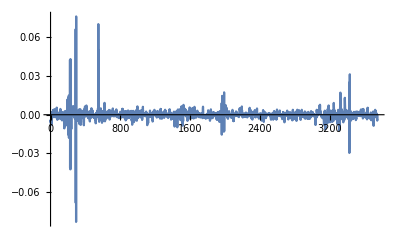

```mathematica
ListLinePlot[rsWethDai, PlotRange->All]
```

```mathematica
edistWethDai = EstimatedDistribution[rsWethDai, StableDistribution[1, aWethDai, bWethDai, locWethDai, scaleWethDai]]
```

StableDistribution[1,1.60712,-0.108702,-0.000176324,0.00134358]

```mathematica
FindDistributionParameters[rsWethDai, StableDistribution[1, aWethDaif, bWethDaif, locWethDaif, scaleWethDaif]]
```

{aWethDaif→1.60712,bWethDaif→-0.108702,locWethDaif→-0.000176324,scaleWethDaif→0.00134358}

```mathematica
(* Not normal ... *)
```

```mathematica
eNormdistWethDai = EstimatedDistribution[rsWethDai, NormalDistribution[uWethDai, sWethDai]]
```

NormalDistribution[-0.000118498,0.00409742]

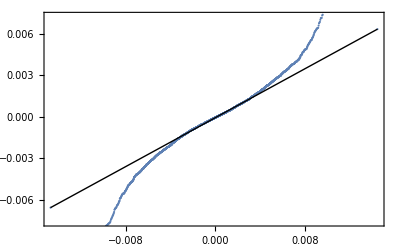

```mathematica
QuantilePlot[rsWethDai]
```

```mathematica
QuantilePlot[rsWethDai, eNormdistWethDai]
```

-Graphics-

```mathematica
(* Stable fit looks good for sample ... *)
```

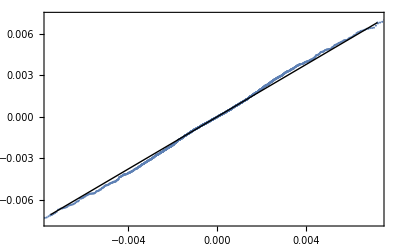

```mathematica
QuantilePlot[rsWethDai, edistWethDai]
```

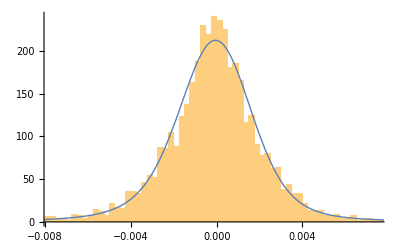

```mathematica
Show[Histogram[rsWethDai, {0.00025}, "PDF"], Plot[PDF[edistWethDai, x], {x, Min[rsWethDai], Max[rsWethDai]}, PlotRange->All, PlotStyle->Thick]]
```

```mathematica
Min[rsWethDai]
```

Log[2322151657675870961664]-Log[2523108235309858422784]

```mathematica
Max[rsWethDai]
```

-Log[2322151657675870961664]+Log[2505792289942667788288]

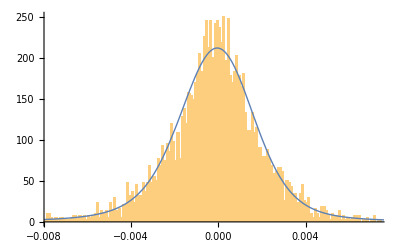

```mathematica
Show[Histogram[rsWethDai, {0.0001}, "PDF"], Plot[PDF[edistWethDai, x], {x, Min[rsWethDai], Max[rsWethDai]}, PlotRange->All, PlotStyle->Thick]]
```

```mathematica
(* Compare the CDFs ... *)
```

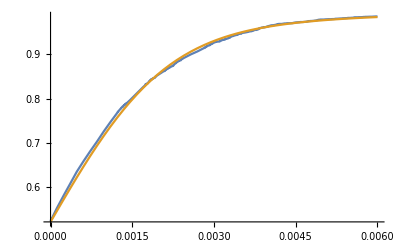

```mathematica
Plot[{CDF[EmpiricalDistribution[rsWethDai],x],CDF[edistWethDai,x]},{x,0,0.006}]
```

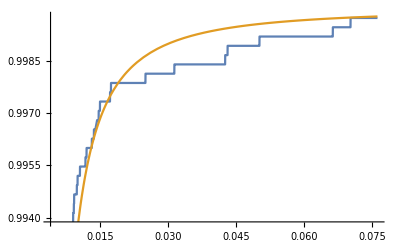

```mathematica
Plot[{CDF[EmpiricalDistribution[rsWethDai],x],CDF[edistWethDai,x]},{x,0.004,Max[rsWethDai]}]
```

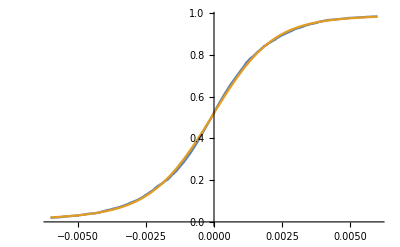

```mathematica
Plot[{CDF[EmpiricalDistribution[rsWethDai],x],CDF[edistWethDai,x]},{x,-0.006,0.006}]
```

```mathematica
(* Look at histogram behavior *)
```

```mathematica
rsWethDai
```

{Log[2807416500389253480448]-Log[2823283256860140896256],Log[2795741643020610568192]-Log[2807416500389253480448],Log[2778509477732340465664]-Log[2795741643020610568192],Log[2767564848768069140480]-Log[2778509477732340465664],Log[2745828354088193490944]-Log[2767564848768069140480],3739,Log[1825074114325430403072]-Log[1832467229514366976000],Log[1817085838281425027072]-Log[1825074114325430403072],Log[1810494773684469760000]-Log[1817085838281425027072],-Log[1810494773684469760000]+Log[1810804556505733136384]}
 |  |  |  |

```mathematica
Length[rsWethDai]
```

3748

```mathematica
(* N rsWethDai obs > 0.001 *)
fGt001= # > 0.001 &;
rsWethDaiGt001 = Select[rsWethDai, fGt001]
```

{-Log[2704041208582260129792]+Log[2708998176205846872064],-Log[2668925655655276085248]+Log[2672304892498461327360],-Log[2671290004550853853184]+Log[2676102749609320251392],-Log[2676102749609320251392]+Log[2680973189376187039744],-Log[2685445606165706702848]+Log[2691518278792935636992],-Log[2691518278792935636992]+Log[2699480089196197052416],-Log[2699480089196197052416]+Log[2708909234860988563456],-Log[2708909234860988563456]+Log[2714017949890912452608],-Log[2714017949890912452608]+Log[2723546549897066446848],-Log[2723546549897066446848]+Log[2728078648189622681600],-Log[2728078648189622681600]+Log[2732798404365623230464],-Log[2732798404365623230464]+Log[2736205750350773747712],-Log[2735655334127838691328]+Log[2741228286855930707968],-Log[2741228286855930707968]+Log[2745848754848815644672],-Log[2745848754848815644672]+Log[2757789870614201761792],-Log[2757789870614201761792]+Log[2762280882964944912384],-Log[2762280882964944912384]+Log[2770548567386833813504],-Log[2770548567386833813504]+Log[2779513401456473931776],-Log[2779513401456473931776]+Log[2783505730499585245184],-Log[2783505730499585245184]+Log[2787899497467968749568],-Log[2787899497467968749568]+Log[2790789899692304498688],-Log[2794184780804205314048]+Log[2799389501740996886528],-Log[2799389501740996886528]+Log[2806764684938647699456],-Log[2806764684938647699456]+Log[2814906782405361664000],-Log[2801977345391733506048]+Log[2807923845137556307968],-Log[2807923845137556307968]+Log[2816680080810950787072],-Log[2816680080810950787072]+Log[2826351345374143184896],-Log[2826351345374143184896]+Log[2829230819690937319424],-Log[2829230819690937319424]+Log[2844881108177347674112],-Log[2847537689695054462976]+Log[2850418206824573960192],-Log[2777110666599693549568]+Log[2781645777707600445440],-Log[2729194017367816404992]+Log[2732073404375411195904],-Log[2732073404375411195904]+Log[2741814525208712183808],-Log[2741814525208712183808]+Log[2754154590660082008064],-Log[2754154590660082008064]+Log[2764600990201965182976],-Log[2764600990201965182976]+Log[2771245643847911342080],-Log[2697833286035274989568]+Log[2702383409000679473152],-Log[2702383409000679473152]+Log[2707925931600913629184],-Log[2707925931600913629184]+Log[2711426836160066355200],-Log[2713939904832290160640]+Log[2717579224720621436928],-Log[2545674672299568005120]+Log[2552634655835315765248],-Log[2552634655835315765248]+Log[2557364095492908122112],-Log[2559261135056533979136]+Log[2561840674093749764096],-Log[2471019747624511602688]+Log[2473771551094868017152],-Log[2474205166847904972800]+Log[2481032975362977431552],-Log[2481032975362977431552]+Log[2488519306973876846592],-Log[2488519306973876846592]+Log[2492668158123786108928],-Log[2494217096224088522752]+Log[2497473160151335174144],-Log[2464500857293495074816]+Log[2470620023525346377728],-Log[2470620023525346377728]+Log[2487411240705092747264],-Log[2487411240705092747264]+Log[2503925670203742486528],-Log[2503925670203742486528]+Log[2533392288718655062016],-Log[2533392288718655062016]+Log[2554130874169823854592],-Log[2554130874169823854592]+Log[2566444149740772786176],-Log[2566444149740772786176]+Log[2574862228426089562112],-Log[2574862228426089562112]+Log[2582260545870247231488],-Log[2582260545870247231488]+Log[2592882335138798108672],-Log[2519054105422384857088]+Log[2553437164742240632832],-Log[2557106974284978847744]+Log[2595501137458207129600],-Log[2491598542381085360128]+Log[2495483668252450619392],-Log[2492649337524945682432]+Log[2600896358324474216448],-Log[2496021223463499857920]+Log[2502102129387371495424],-Log[2502102129387371495424]+Log[2508308939175044317184],-Log[2508308939175044317184]+Log[2517939151397641519104],-Log[2413592805809920671744]+Log[2519753151904606584832],-Log[2363443991403113218048]+Log[2366141807959089872896],-Log[2366141807959089872896]+Log[2370934520687806119936],-Log[2370934520687806119936]+Log[2374631411817024847872],-Log[2374631411817024847872]+Log[2377755789930748968960],-Log[2378498121596980953088]+Log[2383631682552525225984],-Log[2383631682552525225984]+Log[2389372727675175567360],-Log[2389372727675175567360]+Log[2396914492739486744576],-Log[2396914492739486744576]+Log[2405896014948039393280],-Log[2405896014948039393280]+Log[2408807316656603791360],-Log[2408807316656603791360]+Log[2419859296068828135424],-Log[2419859296068828135424]+Log[2427903557470575394816],-Log[2427903557470575394816]+Log[2434682181423286714368],-Log[2434682181423286714368]+Log[2444230879166102765568],-Log[2444230879166102765568]+Log[2460019185309773725696],-Log[2460019185309773725696]+Log[2474184057239067688960],-Log[2474184057239067688960]+Log[2489237812431203336192],-Log[2489237812431203336192]+Log[2505180746918871957504],-Log[2505180746918871957504]+Log[2515657642287079882752],-Log[2515657642287079882752]+Log[2519018250493201743872],-Log[2507491349842502352896]+Log[2511848413215039946752],-Log[2511848413215039946752]+Log[2515511699456128974848],-Log[2498440363433322872832]+Log[2511110178609707352064],-Log[2511110178609707352064]+Log[2519857617219772481536],-Log[2519857617219772481536]+Log[2532161703416493506560],-Log[2532161703416493506560]+Log[2546987349195713675264],-Log[2546987349195713675264]+Log[2556730605436576202752],-Log[2546001124171610849280]+Log[2720404121477766447104],-Log[2322151657675870961664]+Log[2505792289942667788288],-Log[2417609013878362996736]+Log[2420941218413676593152],-Log[2420941218413676593152]+Log[2424258965240024662016],-Log[2424258965240024662016]+Log[2428462021358738472960],-Log[2428462021358738472960]+Log[2431491786797317881856],-Log[2431491786797317881856]+Log[2439317568990628806656],-Log[2368958922356735082496]+Log[2378698763975640219648],-Log[2378698763975640219648]+Log[2381261074101446901760],-Log[2317695470187027365888]+Log[2320361306119120355328],-Log[2320361306119120355328]+Log[2326580013440134807552],-Log[2326580013440134807552]+Log[2336575633208275632128],-Log[2336575633208275632128]+Log[2343571846044937879552],-Log[2228836968636968337408]+Log[2232843070785021542400],-Log[2232843070785021542400]+Log[2236648104912550363136],-Log[2237195445281073659904]+Log[2242680699555422142464],-Log[2242680699555422142464]+Log[2248375923489227145216],-Log[2248375923489227145216]+Log[2253356111269609340928],-Log[2253356111269609340928]+Log[2257170431802223362048],-Log[2257170431802223362048]+Log[2263784536606981488640],-Log[2263784536606981488640]+Log[2268203867222083371008],-Log[2264805976942186070016]+Log[2267152951782084968448],-Log[2267152951782084968448]+Log[2274185225482086121472],-Log[2274185225482086121472]+Log[2280251556297338519552],-Log[2280251556297338519552]+Log[2284257626830097350656],-Log[2214239285407443845120]+Log[2219038517169432821760],-Log[2219038517169432821760]+Log[2228195558270298488832],-Log[2228195558270298488832]+Log[2239727314472643592192],-Log[2239727314472643592192]+Log[2244889727562655989760],-Log[2244889727562655989760]+Log[2259377460932225007616],-Log[2259377460932225007616]+Log[2268323771509710782464],-Log[2268323771509710782464]+Log[2276698677571690954752],-Log[2276698677571690954752]+Log[2280434220083787857920],-Log[2280272596302164918272]+Log[2284672533539892232192],-Log[2284179565280738148352]+Log[2290536927134924144640],-Log[2294068699445464924160]+Log[2301792303038777786368],-Log[2301792303038777786368]+Log[2313127375851468095488],-Log[2313127375851468095488]+Log[2322762095805745070080],-Log[2322762095805745070080]+Log[2332066459418882473984],-Log[2332066459418882473984]+Log[2348825811203421372416],-Log[2348825811203421372416]+Log[2362773749040786964480],-Log[2362773749040786964480]+Log[2375171995237565857792],-Log[2375171995237565857792]+Log[2383735264508229189632],-Log[2383735264508229189632]+Log[2389818086855935000576],-Log[2389818086855935000576]+Log[2399003279267403923456],-Log[2399003279267403923456]+Log[2406177659181134249984],-Log[2406177659181134249984]+Log[2413088879769351094272],-Log[2413088879769351094272]+Log[2418079187044910235648],-Log[2418079187044910235648]+Log[2422923331640665571328],-Log[2422923331640665571328]+Log[2428738583183230500864],-Log[2428738583183230500864]+Log[2433068033040819683328],-Log[2433068033040819683328]+Log[2436728357096947974144],-Log[2436728357096947974144]+Log[2440639857249803042816],-Log[2406936341500033761280]+Log[2409990821034354802688],-Log[2409990821034354802688]+Log[2416132174290223104000],-Log[2416132174290223104000]+Log[2422463985835006492672],-Log[2422463985835006492672]+Log[2426991936485537087488],-Log[2426991936485537087488]+Log[2432516611941791170560],-Log[2359751911227686912000]+Log[2364007131836758097920],-Log[2364007131836758097920]+Log[2368629330499039395840],-Log[2368629330499039395840]+Log[2378065985509337858048],-Log[2378065985509337858048]+Log[2390069350483627081728],-Log[2390069350483627081728]+Log[2394722955101015638016],-Log[2394722955101015638016]+Log[2401283795339037376512],-Log[2401283795339037376512]+Log[2408459189628832317440],-Log[2408459189628832317440]+Log[2411212904729735069696],-Log[2411212904729735069696]+Log[2415056174014640160768],-Log[2417282066002721898496]+Log[2424458019038051172352],-Log[2424458019038051172352]+Log[2428680339574115794944],-Log[2428680339574115794944]+Log[2432196489134873247744],-Log[2432196489134873247744]+Log[2436640247938106261504],-Log[2438850838827532025856]+Log[2446882552339466551296],-Log[2446882552339466551296]+Log[2449959474720159563776],-Log[2302579390120498823168]+Log[2305939123461628362752],-Log[2299830086245623005184]+Log[2302327491702240313344],-Log[2299391258943584468992]+Log[2301733990431579176960],-Log[2301621178760467578880]+Log[2304306096636824911872],-Log[2304306096636824911872]+Log[2310603934131796574208],-Log[2310603934131796574208]+Log[2315559879755051827200],-Log[2315559879755051827200]+Log[2319696790210039250944],-Log[2319696790210039250944]+Log[2322788009533644996608],-Log[2322788009533644996608]+Log[2330389634791029604352],-Log[2330389634791029604352]+Log[2336501601687432331264],-Log[2336501601687432331264]+Log[2345440323437380239360],-Log[2345440323437380239360]+Log[2356976345899373428736],-Log[2356976345899373428736]+Log[2365513621003247812608],-Log[2365513621003247812608]+Log[2384707209845156610048],-Log[2384707209845156610048]+Log[2395965941133844938752],-Log[2395965941133844938752]+Log[2570155672313468551168],-Log[2570155672313468551168]+Log[2574426340567860379648],-Log[2574426340567860379648]+Log[2577297958474596483072],-Log[2577297958474596483072]+Log[2580598572048631463936],-Log[2582923918759191117824]+Log[2715565447663336816640],-Log[2632083320878064467968]+Log[2635492743812619436032],-Log[2635492743812619436032]+Log[2644207014314722721792],-Log[2630558503477801648128]+Log[2635896114941285367808],-Log[2638525968591772188672]+Log[2644120824206141685760],-Log[2644120824206141685760]+Log[2650567972795703099392],-Log[2650567972795703099392]+Log[2659916487470537506816],-Log[2659916487470537506816]+Log[2673114179195965014016],-Log[2673114179195965014016]+Log[2683956717182165975040],-Log[2572058490002816368640]+Log[2576547261802220093440],-Log[2576547261802220093440]+Log[2583835977827362013184],-Log[2583835977827362013184]+Log[2589984876089064816640],-Log[2589984876089064816640]+Log[2596372934966450323456],-Log[2596372934966450323456]+Log[2599300208001102643200],-Log[2599300208001102643200]+Log[2604470050976481411072],-Log[2604470050976481411072]+Log[2608965583553158971392],-Log[2608965583553158971392]+Log[2614262308079360540672],-Log[2561703180254293524480]+Log[2568258804597876850688],-Log[2568258804597876850688]+Log[2577856271758306836480],-Log[2577856271758306836480]+Log[2590063351562627973120],-Log[2590063351562627973120]+Log[2614022428669226516480],-Log[2614022428669226516480]+Log[2621945707621852381184],-Log[2542942782666516201472]+Log[2545945014178631122944],-Log[2545945014178631122944]+Log[2551816519083655954432],-Log[2551816519083655954432]+Log[2555716954514953076736],-Log[2555716954514953076736]+Log[2560249974827626004480],-Log[2560249974827626004480]+Log[2563251352072093696000],-Log[2544843799964662890496]+Log[2549632112590009663488],-Log[2549632112590009663488]+Log[2555072110007625973760],-Log[2555072110007625973760]+Log[2559993476334450900992],-Log[2559993476334450900992]+Log[2562762467649068728320],-Log[2562762467649068728320]+Log[2567383026853496225792],-Log[2567383026853496225792]+Log[2570104632170916610048],-Log[2570960340486723731456]+Log[2573775570396795895808],-Log[2573775570396795895808]+Log[2580955334073237635072],-Log[2580955334073237635072]+Log[2585624186840585601024],-Log[2585821084075665915904]+Log[2589105416686426128384],-Log[2589105416686426128384]+Log[2596543982076617031680],-Log[2596543982076617031680]+Log[2606254834893351026688],-Log[2606254834893351026688]+Log[2613863200457767256064],-Log[2613863200457767256064]+Log[2621283258933720907776],-Log[2564552401229082787840]+Log[2568448436077789184000],-Log[2568448436077789184000]+Log[2574682604010515464192],-Log[2574682604010515464192]+Log[2579605434526716133376],-Log[2579605434526716133376]+Log[2587855810292561739776],-Log[2587855810292561739776]+Log[2596487626709738192896],-Log[2596487626709738192896]+Log[2600408793297687937024],-Log[2600408793297687937024]+Log[2604063351643506212864],-Log[2604063351643506212864]+Log[2609021001067092508672],-Log[2609021001067092508672]+Log[2612930114119166066688],-Log[2612930114119166066688]+Log[2616351596450805710848],-Log[2616351596450805710848]+Log[2619191587591824605184],-Log[2620083646834565185536]+Log[2623237009308826206208],-Log[2619179471029016723456]+Log[2623228233724758851584],-Log[2623228233724758851584]+Log[2627226958497937096704],-Log[2627226958497937096704]+Log[2632371798373776752640],-Log[2632371798373776752640]+Log[2637631444229387976704],-Log[2639960019335621115904]+Log[2643024145488400613376],-Log[2643024145488400613376]+Log[2648965445164438388736],-Log[2648965445164438388736]+Log[2658856923693062291456],-Log[2658856923693062291456]+Log[2671772414101494431744],-Log[2671772414101494431744]+Log[2679241928585557049344],-Log[2679241928585557049344]+Log[2683791894013387735040],-Log[2683791894013387735040]+Log[2688090079455627182080],-Log[2688314968920696553472]+Log[2692520396635379859456],-Log[2679463691638466936832]+Log[2683327949371106394112],-Log[2683327949371106394112]+Log[2686364551382130753536],-Log[2686364551382130753536]+Log[2693080043099917910016],-Log[2693080043099917910016]+Log[2698331561377800388608],-Log[2698331561377800388608]+Log[2702635599349491433472],-Log[2699251230540603326464]+Log[2703857240344843255808],-Log[2703857240344843255808]+Log[2709868450666276454400],-Log[2709868450666276454400]+Log[2716404237381523210240],-Log[2716404237381523210240]+Log[2724403777165872594944],-Log[2724403777165872594944]+Log[2730593507311706177536],-Log[2734382606453125414912]+Log[2743316838597805473792],-Log[2743316838597805473792]+Log[2750925315135166218240],-Log[2750925315135166218240]+Log[2762328823190813409280],-Log[2762328823190813409280]+Log[2773039763521783463936],-Log[2774717755595034722304]+Log[2779074220044939952128],-Log[2692597612352530022400]+Log[2695869970057652076544],-Log[2695869970057652076544]+Log[2702116521682063065088],-Log[2702116521682063065088]+Log[2705765933532933783552],-Log[2705765933532933783552]+Log[2709267648916128006144],-Log[2678335774984018853888]+Log[2684812661346314747904],-Log[2684812661346314747904]+Log[2689044452270794080256],-Log[2689044452270794080256]+Log[2696100835295861145600],-Log[2696100835295861145600]+Log[2702291940650498654208],-Log[2702291940650498654208]+Log[2709241091567094595584],-Log[2709241091567094595584]+Log[2719874817218445312000],-Log[2719874817218445312000]+Log[2725783873484140052480],-Log[2725783873484140052480]+Log[2738473416198420168704],-Log[2738473416198420168704]+Log[2746288987486025678848],-Log[2746288987486025678848]+Log[2754234151564481134592],-Log[2754234151564481134592]+Log[2765982989701810749440],-Log[2765982989701810749440]+Log[2775404424115273072640],-Log[2775404424115273072640]+Log[2784575938540402638848],-Log[2784575938540402638848]+Log[2793798409572372709376],-Log[2793798409572372709376]+Log[2797038221217986772992],-Log[2797038221217986772992]+Log[2802613103337400696832],-Log[2802613103337400696832]+Log[2807410250819032842240],-Log[2807410250819032842240]+Log[2815084253981420027904],-Log[2815084253981420027904]+Log[2821649526109739941888],-Log[2821649526109739941888]+Log[2824890369953852555264],-Log[2824890369953852555264]+Log[2829403940225479081984],-Log[2820080758008356274176]+Log[2824303371074664398848],-Log[2824303371074664398848]+Log[2827426427759331115008],-Log[2827426427759331115008]+Log[2831566641311877431296],-Log[2834271543358982193152]+Log[2837376414485655322624],-Log[2837376414485655322624]+Log[2841241683656176566272],-Log[2841241683656176566272]+Log[2844179489416269004800],-Log[2844179489416269004800]+Log[2849373021065796124672],-Log[2849373021065796124672]+Log[2856015830866606424064],-Log[2856015830866606424064]+Log[2861268159146455728128],-Log[2861268159146455728128]+Log[2868542930345550413824],-Log[2868542930345550413824]+Log[2873664353163396775936],-Log[2873664353163396775936]+Log[2878269371792918839296],-Log[2800352080504099438592]+Log[2807828202021187485696],-Log[2807828202021187485696]+Log[2815800725680400367616],-Log[2815800725680400367616]+Log[2822993854803646873600],-Log[2782202029952323813376]+Log[2786642510601519628288],-Log[2786642510601519628288]+Log[2790276006446543405056],-Log[2790276006446543405056]+Log[2794284413780576698368],-Log[2790747815788384092160]+Log[2793576588354534244352],-Log[2793576588354534244352]+Log[2799513057666381381632],-Log[2799513057666381381632]+Log[2805467344923761049600],-Log[2805467344923761049600]+Log[2814778378464306659328],-Log[2814778378464306659328]+Log[2822283305580246859776],-Log[2822283305580246859776]+Log[2827088354152751300608],-Log[2797328681960259190784]+Log[2803050952204222988288],-Log[2803050952204222988288]+Log[2808946285848189992960],-Log[2808946285848189992960]+Log[2816656477979203338240],-Log[2816656477979203338240]+Log[2819545988447223152640],-Log[2819545988447223152640]+Log[2823729886160320200704],-Log[2820615153010139987968]+Log[2823804013550949105664],-Log[2823804013550949105664]+Log[2826824817411424256000],-Log[2826824817411424256000]+Log[2830077430587885355008],-Log[2832849080820258308096]+Log[2836516060133680218112],-Log[2836516060133680218112]+Log[2845046041733353177088],-Log[2845046041733353177088]+Log[2849645424714348756992],-Log[2714431254502593527808]+Log[2720120309083598749696],-Log[2720120309083598749696]+Log[2726364775644996829184],-Log[2726364775644996829184]+Log[2731961272919092887552],-Log[2731961272919092887552]+Log[2739218376251850358784],-Log[2739218376251850358784]+Log[2743120416675640377344],-Log[2743120416675640377344]+Log[2751373727214955134976],-Log[2615618176938780131328]+Log[2619508040157724409856],-Log[2622297698169066094592]+Log[2625108778696560345088],-Log[2624006751375628697600]+Log[2628004046914858254336],-Log[2628004046914858254336]+Log[2636820241750474883072],-Log[2636820241750474883072]+Log[2644249605412866752512],-Log[2644249605412866752512]+Log[2648948571941968543744],-Log[2593067839944002633728]+Log[2597308929097398747136],-Log[2597308929097398747136]+Log[2608852971672587730944],-Log[2608852971672587730944]+Log[2622525710093482721280],-Log[2622525710093482721280]+Log[2639534541706350297088],-Log[2639534541706350297088]+Log[2645508657392803381248],-Log[2633179387986335760384]+Log[2638148422514275516416],-Log[2638148422514275516416]+Log[2641445316995047751680],-Log[2641445316995047751680]+Log[2644980232469751005184],-Log[2648739671947223760896]+Log[2654804054872351047680],-Log[2654804054872351047680]+Log[2659605625232196894720],-Log[2659605625232196894720]+Log[2664184637349025546240],-Log[2664184637349025546240]+Log[2667850311140343021568],-Log[2667039761401466847232]+Log[2672347297817941245952],-Log[2672347297817941245952]+Log[2679974222071630135296],-Log[2679974222071630135296]+Log[2688030022035024379904],-Log[2688030022035024379904]+Log[2693758389024537444352],-Log[2691451574454483156992]+Log[2694752877526071115776],-Log[2689060928474332528640]+Log[2693690162161369743360],-Log[2693690162161369743360]+Log[2699350857103040839680],-Log[2699350857103040839680]+Log[2705721505402915389440],-Log[2705721505402915389440]+Log[2709063183236070375424],-Log[2709063183236070375424]+Log[2718936884886513909760],-Log[2718936884886513909760]+Log[2724281242538555736064],-Log[2680837503199937560576]+Log[2688535102126789492736],-Log[2688535102126789492736]+Log[2698345376632750997504],-Log[2698345376632750997504]+Log[2707812329822851956736],-Log[2707812329822851956736]+Log[2717888804620991987712],-Log[2717888804620991987712]+Log[2734686794573074137088],-Log[2734686794573074137088]+Log[2743059798661351866368],-Log[2743059798661351866368]+Log[2752105502350137360384],-Log[2752105502350137360384]+Log[2755797345400431050752],-Log[2773675547628049793024]+Log[2777198899141338988544],-Log[2777198899141338988544]+Log[2781173246166026944512],-Log[2781173246166026944512]+Log[2787919873151630573568],-Log[2787919873151630573568]+Log[2791188780501537652736],-Log[2791544841467622064128]+Log[2794467353276905947136],-Log[2794467353276905947136]+Log[2798285454632618557440],-Log[2605269200310611476480]+Log[2613619098950207799296],-Log[2613619098950207799296]+Log[2621958131420375285760],-Log[2621958131420375285760]+Log[2629780661609822683136],-Log[2629780661609822683136]+Log[2633732350429349019648],-Log[2620027072757396144128]+Log[2624112404092066725888],-Log[2569468233822292672512]+Log[2572435217228513673216],-Log[2575405095932781395968]+Log[2578174202102379708416],-Log[2578174202102379708416]+Log[2580754406509080739840],-Log[2583121301858383036416]+Log[2588998502044324069376],-Log[2588998502044324069376]+Log[2596151047977263693824],-Log[2596151047977263693824]+Log[2603244954086065831936],-Log[2603244954086065831936]+Log[2609948133392020668416],-Log[2609948133392020668416]+Log[2617591258532937203712],-Log[2617591258532937203712]+Log[2623383067156287062016],-Log[2625069888654662434816]+Log[2629994022251346264064],-Log[2629994022251346264064]+Log[2636435943905350385664],-Log[2636435943905350385664]+Log[2642803444718302658560],-Log[2642803444718302658560]+Log[2652868266916373856256],-Log[2652868266916373856256]+Log[2660413794848968540160],-Log[2660413794848968540160]+Log[2666812281636131438592],-Log[2666812281636131438592]+Log[2669942768531790102528],-Log[2669942768531790102528]+Log[2674883313630384750592],-Log[2674883313630384750592]+Log[2677909780179792166912],-Log[2678878537409630306304]+Log[2681833982027587125248],-Log[2661988284927158779904]+Log[2665549973287005061120],-Log[2665549973287005061120]+Log[2669215500132935008256],-Log[2669215500132935008256]+Log[2674118424782762409984],-Log[2674118424782762409984]+Log[2681454677656785649664],-Log[2681454677656785649664]+Log[2688733379286913253376],-Log[2688733379286913253376]+Log[2696536271202404532224],-Log[2696536271202404532224]+Log[2701592000713647456256],-Log[2701592000713647456256]+Log[2707983771105833254912],-Log[2707983771105833254912]+Log[2714089583509649752064],-Log[2716409119397917491200]+Log[2720553759460491264000],-Log[2720553759460491264000]+Log[2723569866302833557504],-Log[2723569866302833557504]+Log[2726333211622327713792],-Log[2666041919148028067840]+Log[2669388580037979537408],-Log[2669388580037979537408]+Log[2678608684261605638144],-Log[2678608684261605638144]+Log[2690774761233281187840],-Log[2690774761233281187840]+Log[2698725897796276715520],-Log[2698725897796276715520]+Log[2710453182245971689472],-Log[2710453182245971689472]+Log[2715156279961744048128],-Log[2679906988766092328960]+Log[2683174983925048016896],-Log[2683174983925048016896]+Log[2688556835436257869824],-Log[2688556835436257869824]+Log[2693737429284208246784],-Log[2693737429284208246784]+Log[2699620327316393033728],-Log[2699620327316393033728]+Log[2703256157160689106944],-Log[2686536092659138691072]+Log[2689427374118231080960],-Log[2689427374118231080960]+Log[2693309663507626065920],-Log[2693309663507626065920]+Log[2696244234897789026304],-Log[2697928679815854424064]+Log[2706737229682764677120],-Log[2706737229682764677120]+Log[2714150319476261781504],-Log[2714150319476261781504]+Log[2723004391884826083328],-Log[2723004391884826083328]+Log[2732585657129100640256],-Log[2732585657129100640256]+Log[2743140383608634605568],-Log[2743140383608634605568]+Log[2746995323397418778624],-Log[2751482994025877733376]+Log[2756259043327769837568],-Log[2756259043327769837568]+Log[2761197309679982084096],-Log[2761197309679982084096]+Log[2767482709501035937792],-Log[2767482709501035937792]+Log[2775620288131434020864],-Log[2775620288131434020864]+Log[2782442315195442266112],-Log[2754482268930942959616]+Log[2757321468672492961792],-Log[2754733344398484439040]+Log[2758332799846182813696],-Log[2758332799846182813696]+Log[2763804017556298137600],-Log[2763804017556298137600]+Log[2770837445431034118144],-Log[2770837445431034118144]+Log[2779976201974185459712],-Log[2779976201974185459712]+Log[2789193293235395493888],-Log[2789193293235395493888]+Log[2801128341106827198464],-Log[2801128341106827198464]+Log[2808679628154843168768],-Log[2808679628154843168768]+Log[2818346104402279923712],-Log[2818346104402279923712]+Log[2821672805533246029824],-Log[2819767433382336659456]+Log[2824648723826162008064],-Log[2695343281551967256576]+Log[2699158801191407190016],-Log[2699158801191407190016]+Log[2705425587724472025088],-Log[2705425587724472025088]+Log[2711907263701455994880],-Log[2711907263701455994880]+Log[2715876281149443538944],-Log[2604098065338088816640]+Log[2607273971367855783936],-Log[2607273971367855783936]+Log[2611078763289598492672],-Log[2613374253649909776384]+Log[2616171191241508651008],-Log[2580765949066344923136]+Log[2588143139542656876544],-Log[2588143139542656876544]+Log[2593688367211491622912],-Log[2593688367211491622912]+Log[2597898520074588782592],-Log[2477143930296823971840]+Log[2480110203360453328896],-Log[2480110203360453328896]+Log[2488489496657328603136],-Log[2488489496657328603136]+Log[2498570991723067473920],-Log[2498570991723067473920]+Log[2504189872401904828416],-Log[2484958538470870482944]+Log[2487812994433725497344],-Log[2478274735240447000576]+Log[2481038045892072439808],-Log[2481038045892072439808]+Log[2486256636595084460032],-Log[2486256636595084460032]+Log[2488984735388365488128],-Log[2488984735388365488128]+Log[2499426888782963015680],-Log[2499426888782963015680]+Log[2509439788361951739904],-Log[2509439788361951739904]+Log[2517257645371946434560],-Log[2517257645371946434560]+Log[2523134687654517407744],-Log[2523134687654517407744]+Log[2528042168272334880768],-Log[2528042168272334880768]+Log[2535724252469113913344],-Log[2535724252469113913344]+Log[2538436778314013081600],-Log[2491854285040702717952]+Log[2507551882221181206528],-Log[2496711008282012549120]+Log[2501761732134535954432],-Log[2501761732134535954432]+Log[2508163675337690972160],-Log[2508163675337690972160]+Log[2512475813948814262272],-Log[2502653781183760433152]+Log[2518537697478862438400],-Log[2348612326403148087296]+Log[2366628601682375737344],-Log[2366628601682375737344]+Log[2382992524166543441920],-Log[2382992524166543441920]+Log[2396301460342430498816],-Log[2396301460342430498816]+Log[2402643543703078567936],-Log[2403825134587114160128]+Log[2407131710994063556608],-Log[2407131710994063556608]+Log[2414632174273932296192],-Log[2414632174273932296192]+Log[2422201395074361720832],-Log[2422201395074361720832]+Log[2433782724341738242048],-Log[2433782724341738242048]+Log[2443876961684248592384],-Log[2443876961684248592384]+Log[2453561422377404858368],-Log[2453561422377404858368]+Log[2460351843317494317056],-Log[2460351843317494317056]+Log[2465582073888661045248],-Log[2465582073888661045248]+Log[2470778190016284196864],-Log[2470778190016284196864]+Log[2475397574018373517312],-Log[2475397574018373517312]+Log[2479018616298130636800],-Log[2479018616298130636800]+Log[2482070399460519182336],-Log[2482070399460519182336]+Log[2487430130832096886784],-Log[2487430130832096886784]+Log[2493241935570598363136],-Log[2493241935570598363136]+Log[2497524052013556432896],-Log[2497524052013556432896]+Log[2507422984204870746112],-Log[2507422984204870746112]+Log[2513436429239923507200],-Log[2513436429239923507200]+Log[2520058147437240385536],-Log[2520058147437240385536]+Log[2525852057666254274560],-Log[2520918538207370412032]+Log[2528155368253980934144],-Log[2435117952973741228032]+Log[2438575904260244897792],-Log[2438575904260244897792]+Log[2441077433090166489088],-Log[2441077433090166489088]+Log[2446950846136215142400],-Log[2446950846136215142400]+Log[2453928935992780652544],-Log[2434726148406491217920]+Log[2438124883911341244416],-Log[2438124883911341244416]+Log[2451952781382999605248],-Log[2451952781382999605248]+Log[2461782103482311901184],-Log[2461782103482311901184]+Log[2471587102789929009152],-Log[2471587102789929009152]+Log[2476819475278487093248],-Log[2481037246009815597056]+Log[2486576430232524292096],-Log[2486576430232524292096]+Log[2494839422131180666880],-Log[2494839422131180666880]+Log[2504086698756340187136],-Log[2504086698756340187136]+Log[2516879610035470598144],-Log[2516879610035470598144]+Log[2524377979365657935872],-Log[2489810105132828327936]+Log[2492539245827634233344],-Log[2492539245827634233344]+Log[2497336353812403716096],-Log[2497336353812403716096]+Log[2500469050759172849664],-Log[2501389465311134613504]+Log[2506172241509608325120],-Log[2506172241509608325120]+Log[2519250618880464257024],-Log[2519250618880464257024]+Log[2530085595225515884544],-Log[2530085595225515884544]+Log[2542019538942447583232],-Log[2542019538942447583232]+Log[2553365122868209778688],-Log[2553365122868209778688]+Log[2557159932978146050048],-Log[2513338576424460091392]+Log[2522849886810853605376],-Log[2522849886810853605376]+Log[2532971263803778924544],-Log[2532971263803778924544]+Log[2548533600473808633856],-Log[2548533600473808633856]+Log[2560197310019780214784],-Log[2560197310019780214784]+Log[2564331643884112707584],-Log[2564331643884112707584]+Log[2568866731829282996224],-Log[2568866731829282996224]+Log[2573627219701312520192],-Log[2573627219701312520192]+Log[2582681373442609512448],-Log[2582681373442609512448]+Log[2588989480751558295552],-Log[2588989480751558295552]+Log[2594847189266609995776],-Log[2594847189266609995776]+Log[2600460582749137797120],-Log[2568359904054436429824]+Log[2571319406111576555520],-Log[2571319406111576555520]+Log[2577106531049735192576],-Log[2577106531049735192576]+Log[2585153278938502922240],-Log[2585153278938502922240]+Log[2591423645836966363136],-Log[2591423645836966363136]+Log[2595701583839957614592],-Log[2595701583839957614592]+Log[2600467971739120828416],-Log[2570988713617032478720]+Log[2573662489263730589696],-Log[2573662489263730589696]+Log[2576666289816529272832],-Log[2533374725957637111808]+Log[2536167186739328188416],-Log[2512257688511253053440]+Log[2516343022877865410560],-Log[2516343022877865410560]+Log[2522590893984695451648],-Log[2522590893984695451648]+Log[2534970445740011683840],-Log[2534970445740011683840]+Log[2548395363083930828800],-Log[2548395363083930828800]+Log[2564306014270758322176],-Log[2564306014270758322176]+Log[2576491308088262393856],-Log[2576491308088262393856]+Log[2583222998425563824128],-Log[2583222998425563824128]+Log[2586118065138723454976],-Log[2440338384611831185408]+Log[2445437489475202056192],-Log[2445437489475202056192]+Log[2453861247624948482048],-Log[2453861247624948482048]+Log[2459627479137708408832],-Log[2459627479137708408832]+Log[2462472708758009020416],-Log[2464853537829883478016]+Log[2469410921434184155136],-Log[2469410921434184155136]+Log[2472863124072246018048],-Log[2475124343020938330112]+Log[2477791132979844612096],-Log[2419348917729162166272]+Log[2422088576662671720448],-Log[2422088576662671720448]+Log[2432196574945185628160],-Log[2432196574945185628160]+Log[2440368301073036738560],-Log[2440368301073036738560]+Log[2445862403295011667968],-Log[2445862403295011667968]+Log[2450261906188835749888],-Log[2450261906188835749888]+Log[2454185328068284383232],-Log[2459119356399121858560]+Log[2462120207864398610432],-Log[2462120207864398610432]+Log[2466001271517989568512],-Log[2468291537339134509056]+Log[2471253676502551101440],-Log[2431572931894137847808]+Log[2435446113711717613568],-Log[2435446113711717613568]+Log[2440165729310042750976],-Log[2440165729310042750976]+Log[2445094870909333274624],-Log[2445094870909333274624]+Log[2448946808128090406912],-Log[2448946808128090406912]+Log[2452068624463493595136],-Log[2451425332608609812480]+Log[2455545885682257887232],-Log[2457945492051718569984]+Log[2460839680052621213696],-Log[2460839680052621213696]+Log[2463673226468565975040],-Log[2465077006465526398976]+Log[2468576344861920722944],-Log[2382379008547950690304]+Log[2385561930114712207360],-Log[2385561930114712207360]+Log[2389391227031845339136],-Log[2389391227031845339136]+Log[2394292000312850382848],-Log[2397500082573699186688]+Log[2401858299841327661056],-Log[2401858299841327661056]+Log[2404398329259763433472],-Log[2344145169850599735296]+Log[2350781728577335853056],-Log[2350781728577335853056]+Log[2356748685670191988736],-Log[2356748685670191988736]+Log[2361289001955971563520],-Log[2297231270768012689408]+Log[2317956463755289952256],-Log[2251663575451959820288]+Log[2284843636842982014976],-Log[2286332330263843176448]+Log[2290147302710132867072],-Log[2257341702714195968000]+Log[2289155893736853733376],-Log[2289155893736853733376]+Log[2294639013656889917440],-Log[2296350715016861188096]+Log[2302931843464126791680],-Log[2302931843464126791680]+Log[2343196769077410398208],-Log[2316782148458734682112]+Log[2325870650889875488768],-Log[2325870650889875488768]+Log[2338881278814636474368],-Log[2338881278814636474368]+Log[2352434668930192375808],-Log[2352434668930192375808]+Log[2360557288651100520448],-Log[2360557288651100520448]+Log[2377968891920638279680],-Log[2377968891920638279680]+Log[2382094807344667951104],-Log[2380537895838419517440]+Log[2383752927227781578752],-Log[2383752927227781578752]+Log[2390343820483261628416],-Log[2390343820483261628416]+Log[2398610992079086026752],-Log[2398610992079086026752]+Log[2411736868485627117568],-Log[2411736868485627117568]+Log[2422499958241165836288],-Log[2422499958241165836288]+Log[2427932186610769068032],-Log[2427932186610769068032]+Log[2433242350818182561792],-Log[2388471972081522704384]+Log[2391402512018200592384],-Log[2391402512018200592384]+Log[2398051037499552169984],-Log[2398051037499552169984]+Log[2402340884118531211264],-Log[2402340884118531211264]+Log[2407292645677784367104],-Log[2407292645677784367104]+Log[2410438373390285275136],-Log[2363999904021892038656]+Log[2370289455969571700736],-Log[2370289455969571700736]+Log[2377680789821001826304],-Log[2377680789821001826304]+Log[2385805411600817455104],-Log[2385805411600817455104]+Log[2394835918266787954688],-Log[2394835918266787954688]+Log[2401960748242684608512],-Log[2320987167774208163840]+Log[2323727519154435522560],-Log[2323727519154435522560]+Log[2326690365104277684224],-Log[2326690365104277684224]+Log[2329063014288573333504],-Log[2331503288924217540608]+Log[2335415478621047095296],-Log[2335415478621047095296]+Log[2339610336510753374208],-Log[2339610336510753374208]+Log[2345610524250355531776],-Log[2345610524250355531776]+Log[2350308820151775789056],-Log[2353152074477118685184]+Log[2357472924619646959616],-Log[2357472924619646959616]+Log[2360210955640015421440],-Log[2360210955640015421440]+Log[2363663231382906208256],-Log[2340076655942312656896]+Log[2345834842157864714240],-Log[2345834842157864714240]+Log[2357458987318724788224],-Log[2357458987318724788224]+Log[2368573585971598065664],-Log[2368573585971598065664]+Log[2377214890177686142976],-Log[2377214890177686142976]+Log[2388342382966828171264],-Log[2388342382966828171264]+Log[2393436048238520041472],-Log[2396088804457371926528]+Log[2398705255545287737344],-Log[2398705255545287737344]+Log[2402867302821856804864],-Log[2402867302821856804864]+Log[2408314082983007485952],-Log[2408314082983007485952]+Log[2414284552587573198848],-Log[2414284552587573198848]+Log[2418058228141873692672],-Log[2418058228141873692672]+Log[2424911673547283759104],-Log[2424911673547283759104]+Log[2428744453260266962944],-Log[2427432762981596790784]+Log[2431941434237457006592],-Log[2431941434237457006592]+Log[2440621916268867354624],-Log[2440621916268867354624]+Log[2452563767603314556928],-Log[2452563767603314556928]+Log[2464181026182759186432],-Log[2464181026182759186432]+Log[2477542467403152097280],-Log[2477542467403152097280]+Log[2493424810877675634688],-Log[2493424810877675634688]+Log[2501245694828405587968],-Log[2501245694828405587968]+Log[2509653596233692872704],-Log[2509653596233692872704]+Log[2518166422013235691520],-Log[2518166422013235691520]+Log[2523860847546841169920],-Log[2478096316457532522496]+Log[2480578504953053577216],-Log[2480578504953053577216]+Log[2484797222494756929536],-Log[2484797222494756929536]+Log[2488933147512751521792],-Log[2488933147512751521792]+Log[2492974424888487444480],-Log[2492974424888487444480]+Log[2495651751355681341440],-Log[2475181810362676150272]+Log[2478790435789827735552],-Log[2478790435789827735552]+Log[2481596500897614004224],-Log[2482612945887634128896]+Log[2485778046853169807360],-Log[2485778046853169807360]+Log[2493359478638561460224],-Log[2493359478638561460224]+Log[2503436814681293455360],-Log[2503436814681293455360]+Log[2512765727459969597440],-Log[2512765727459969597440]+Log[2526264457501437591552],-Log[2526264457501437591552]+Log[2537682378991934111744],-Log[2537682378991934111744]+Log[2544529767544621367296],-Log[2544529767544621367296]+Log[2551267758626673000448],-Log[2551267758626673000448]+Log[2556900266627319726080],-Log[2556900266627319726080]+Log[2559892639922630688768],-Log[2559892639922630688768]+Log[2562706220786057216000],-Log[2557145363974239289344]+Log[2560894894793317416960],-Log[2560894894793317416960]+Log[2566735249587334283264],-Log[2566735249587334283264]+Log[2575578488125212590080],-Log[2575578488125212590080]+Log[2579917365599030214656],-Log[2529196638229669347328]+Log[2532173435592398864384],-Log[2535015766749390307328]+Log[2538965998147082387456],-Log[2538965998147082387456]+Log[2544161514910479024128],-Log[2544161514910479024128]+Log[2547221051904703332352],-Log[2547221051904703332352]+Log[2552795439521447542784],-Log[2552795439521447542784]+Log[2556682657295933898752],-Log[2556682657295933898752]+Log[2560512751274832166912],-Log[2562964456450049441792]+Log[2566158126262354706432],-Log[2566158126262354706432]+Log[2570120001449443196928],-Log[2570120001449443196928]+Log[2575989296142711521280],-Log[2575989296142711521280]+Log[2582380957893541232640],-Log[2582380957893541232640]+Log[2591752163063445848064],-Log[2591752163063445848064]+Log[2598794118000184131584],-Log[2598794118000184131584]+Log[2604017369671413530624],-Log[2589023143021684195328]+Log[2592112237593562185728],-Log[2592112237593562185728]+Log[2600666166161482711040],-Log[2602669752218502561792]+Log[2615301031361771995136],-Log[2615301031361771995136]+Log[2620032670279584972800],-Log[2582076122459576205312]+Log[2585074576467192971264],-Log[2585074576467192971264]+Log[2587820545134016593920],-Log[2544872986164929757184]+Log[2547723739937236844544],-Log[2547723739937236844544]+Log[2550904580227885170688],-Log[2555329041664482213888]+Log[2559958030789934841856],-Log[2559958030789934841856]+Log[2568770890373535891456],-Log[2568770890373535891456]+Log[2577014893729980874752],-Log[2577014893729980874752]+Log[2583772876460291784704],-Log[2583772876460291784704]+Log[2591948793667339681792],-Log[2531933709110680223744]+Log[2535711914907963228160],-Log[2535711914907963228160]+Log[2538592694252148359168],-Log[2538592694252148359168]+Log[2543206205506828369920],-Log[2543206205506828369920]+Log[2546875333118797021184],-Log[2546875333118797021184]+Log[2549924857123953442816],-Log[2549924857123953442816]+Log[2552546360928476069888],-Log[2521141456453007572992]+Log[2523677791908668112896],-Log[2527758815382708158464]+Log[2530877034515198902272],-Log[2530877034515198902272]+Log[2534153437851767799808],-Log[2536116131914570530816]+Log[2538953603211352604672],-Log[2417105356922699120640]+Log[2421218394986763517952],-Log[2421218394986763517952]+Log[2423676009010388008960],-Log[2400518260887749918720]+Log[2403945579768753160192],-Log[2403945579768753160192]+Log[2410854830875643740160],-Log[2404540358615555375104]+Log[2408157426831598813184],-Log[2408157426831598813184]+Log[2413244432407128440832],-Log[2413244432407128440832]+Log[2418824442763587092480],-Log[2362304428409018646528]+Log[2365853290547393855488],-Log[2365853290547393855488]+Log[2375384141844205535232],-Log[2375384141844205535232]+Log[2381749046871664361472],-Log[2381749046871664361472]+Log[2386543767305620815872],-Log[2386543767305620815872]+Log[2389305713648960274432],-Log[2389305713648960274432]+Log[2393185768258787606528],-Log[2393185768258787606528]+Log[2395978723919891267584],-Log[2403058047770304708608]+Log[2408299865642156163072],-Log[2408299865642156163072]+Log[2411369955389236838400],-Log[2411369955389236838400]+Log[2413832980386044968960],-Log[2413832980386044968960]+Log[2416704283669977628672],-Log[2416704283669977628672]+Log[2419301584871590723584],-Log[2419301584871590723584]+Log[2422313894783484428288],-Log[2422313894783484428288]+Log[2425497023992327831552],-Log[2423335677241236914176]+Log[2426458704851775258624],-Log[2426458704851775258624]+Log[2429457588807625342976],-Log[2429457588807625342976]+Log[2437419465754499612672],-Log[2437419465754499612672]+Log[2441314571338505519104],-Log[2441314571338505519104]+Log[2445171623169731067904],-Log[2377492493151350816768]+Log[2381501849826604613632],-Log[2381501849826604613632]+Log[2385118881292987400192],-Log[2385118881292987400192]+Log[2390019036151319363584],-Log[2390019036151319363584]+Log[2393665366325820653568],-Log[2393665366325820653568]+Log[2397950969953289502720],-Log[2325841098319259762688]+Log[2328201093585958862848],-Log[2330119055806081269760]+Log[2333555269439726026752],-Log[2334294788622286848000]+Log[2337511476629581070336],-Log[2340236481837175144448]+Log[2343100113342921179136],-Log[2343100113342921179136]+Log[2350600564371684851712],-Log[2350600564371684851712]+Log[2355623946786546647040],-Log[2355623946786546647040]+Log[2360976672443683569664],-Log[2360976672443683569664]+Log[2365550615463557857280],-Log[2326787192779549966336]+Log[2329211504249137790976],-Log[2329211504249137790976]+Log[2332835792555472846848],-Log[2332835792555472846848]+Log[2336193784467263848448],-Log[2345879919390421417984]+Log[2348483456666551713792],-Log[2348483456666551713792]+Log[2353204957485788299264],-Log[2353204957485788299264]+Log[2355939157067044487168],-Log[2334134683796286996480]+Log[2336709864210677891072],-Log[2336709864210677891072]+Log[2339965095137846231040],-Log[2339965095137846231040]+Log[2342700295542581493760],-Log[2300133415951640559616]+Log[2303168887530914578432],-Log[2303168887530914578432]+Log[2308482742502184452096],-Log[2308482742502184452096]+Log[2314524799629592100864],-Log[2314524799629592100864]+Log[2323421070461381115904],-Log[2219358158015192104960]+Log[2224506991405732986880],-Log[2224506991405732986880]+Log[2227906795942382927872],-Log[2156335241127807942656]+Log[2160089703034393198592],-Log[2160089703034393198592]+Log[2165102446743694606336],-Log[2165102446743694606336]+Log[2173514699124391542784],-Log[2173514699124391542784]+Log[2180553513208027283456],-Log[2180553513208027283456]+Log[2186202827932464840704],-Log[2186202827932464840704]+Log[2189696994890416128000],-Log[2189696994890416128000]+Log[2192578802733275676672],-Log[2192967493681432231936]+Log[2195771452015102656512],-Log[2195771452015102656512]+Log[2201746941898948608000],-Log[2201746941898948608000]+Log[2205310679395061989376],-Log[2205310679395061989376]+Log[2207520259568651993088],-Log[2206998487307934760960]+Log[2211234973611542446080],-Log[2211234973611542446080]+Log[2214237726286333870080],-Log[2214237726286333870080]+Log[2218127067532633309184],-Log[2218127067532633309184]+Log[2223882882382057177088],-Log[2223882882382057177088]+Log[2231578314778018840576],-Log[2231578314778018840576]+Log[2235145684864934608896],-Log[2237348475130157203456]+Log[2239836575353958825984],-Log[2185941113547133288448]+Log[2189356145106427838464],-Log[2189356145106427838464]+Log[2192209115844879319040],-Log[2193379606412804489216]+Log[2197096919043153854464],-Log[2197096919043153854464]+Log[2201789227885787086848],-Log[2201789227885787086848]+Log[2206013548065239334912],-Log[2206013548065239334912]+Log[2212159971734142320640],-Log[2212159971734142320640]+Log[2220656400798023680000],-Log[2220656400798023680000]+Log[2228979870508082528256],-Log[2228979870508082528256]+Log[2234714723049249701888],-Log[2236924441741051822080]+Log[2239599730447567290368],-Log[2230580496599392452608]+Log[2233162589794864201728],-Log[2233162589794864201728]+Log[2235906808294407143424],-Log[2229812138088804646912]+Log[2233556287458397388800],-Log[2233556287458397388800]+Log[2239226587359581044736],-Log[2239226587359581044736]+Log[2244875565258525638656],-Log[2244875565258525638656]+Log[2250173947108628103168],-Log[2233762451673390776320]+Log[2236047698697764208640],-Log[2236047698697764208640]+Log[2239321738589601792000],-Log[2239321738589601792000]+Log[2243094563646412161024],-Log[2243094563646412161024]+Log[2245659036874993041408],-Log[2200041413573150244864]+Log[2203174847171920134144],-Log[2203174847171920134144]+Log[2207993030917184552960],-Log[2207993030917184552960]+Log[2210658640444770222080],-Log[2210658640444770222080]+Log[2214604546878137958400],-Log[2214604546878137958400]+Log[2216936683623703117824],-Log[2156714030279222362112]+Log[2161158930747023163392],-Log[2161158930747023163392]+Log[2167245529247265062912],-Log[2167245529247265062912]+Log[2171757228507484389376],-Log[2171757228507484389376]+Log[2175100567072572964864],-Log[2166094595280540532736]+Log[2168827241651821608960],-Log[2170810556816610295808]+Log[2175110632036161290240],-Log[2175110632036161290240]+Log[2179028948756767440896],-Log[2183630395753879044096]+Log[2187589605852449865728],-Log[2187589605852449865728]+Log[2190623146395665170432],-Log[2190623146395665170432]+Log[2193384936658262556672],-Log[2193384936658262556672]+Log[2197505429300083425280],-Log[2060198210246686801920]+Log[2067573301732184948736],-Log[2067573301732184948736]+Log[2075492392421695160320],-Log[2075492392421695160320]+Log[2080362689994931830784],-Log[2080362689994931830784]+Log[2084065563873602961408],-Log[2085862993968969809920]+Log[2092805669042672107520],-Log[2092805669042672107520]+Log[2098219569107741704192],-Log[2098219569107741704192]+Log[2101767896693492678656],-Log[2101767896693492678656]+Log[2109140352211587956736],-Log[2109140352211587956736]+Log[2112301185676543787008],-Log[2117563900033907032064]+Log[2119744770443303976960],-Log[2126170259330304835584]+Log[2128605283723410931712],-Log[2132854364855865180160]+Log[2135719955959677452288],-Log[2135719955959677452288]+Log[2139437681862839894016],-Log[2139437681862839894016]+Log[2144475700041591029760],-Log[2144475700041591029760]+Log[2151146905531733770240],-Log[2151146905531733770240]+Log[2158361051818513661952],-Log[2158361051818513661952]+Log[2174406279221437267968],-Log[2174406279221437267968]+Log[2186101687954426822656],-Log[2186101687954426822656]+Log[2194953645109268971520],-Log[2194953645109268971520]+Log[2211958331007524143104],-Log[2211958331007524143104]+Log[2227568101164274941952],-Log[2227568101164274941952]+Log[2232652972962988687360],-Log[2232652972962988687360]+Log[2239650895323576664064],-Log[2239650895323576664064]+Log[2246139219985038835712],-Log[2248734204989101309952]+Log[2251585814937031147520],-Log[2251585814937031147520]+Log[2253903348784891428864],-Log[2098878851789449068544]+Log[2103206854137903579136],-Log[2103206854137903579136]+Log[2106740719525263048704],-Log[2107693891218991742976]+Log[2114341673986911633408],-Log[2114341673986911633408]+Log[2120156293355021795328],-Log[2005610473326967521280]+Log[2008743226711612325888],-Log[2008743226711612325888]+Log[2011573135049808412672],-Log[2011573135049808412672]+Log[2014273941310535630848],-Log[1999478785841335894016]+Log[2001841661593928335360],-Log[1930917562836760920064]+Log[1936630470475625267200],-Log[1936630470475625267200]+Log[1943425464510525997056],-Log[1943425464510525997056]+Log[1952164823813168824320],-Log[1952164823813168824320]+Log[1957667765136068182016],-Log[1957667765136068182016]+Log[1961501645669415256064],-Log[1946643881566086889472]+Log[1949772615635500531712],-Log[1949772615635500531712]+Log[1960671298477818380288],-Log[1960671298477818380288]+Log[1974795478613198110720],-Log[1974795478613198110720]+Log[1981475345522907414528],-Log[1981475345522907414528]+Log[1986465808227539091456],-Log[1986465808227539091456]+Log[1992296361758360076288],-Log[1992296361758360076288]+Log[1994369179071748505600],-Log[1993222804971587371008]+Log[1996430292720002007040],-Log[1928775430174837571584]+Log[1931036091947649597440],-Log[1925011119047286718464]+Log[1931269126177116913664],-Log[1931269126177116913664]+Log[1936579389659636826112],-Log[1936579389659636826112]+Log[1941658410818633465856],-Log[1941658410818633465856]+Log[1945567016217649872896],-Log[1934327409461798633472]+Log[1937701978482341314560],-Log[1937701978482341314560]+Log[1940890058236229844992],-Log[1882701688159702876160]+Log[1888901365522582994944],-Log[1888901365522582994944]+Log[1894444822572797526016],-Log[1894444822572797526016]+Log[1897646667973494046720],-Log[1883562226553717784576]+Log[1888260842836997439488],-Log[1888260842836997439488]+Log[1901818121902213562368],-Log[1901818121902213562368]+Log[1919278395407136456704],-Log[1919278395407136456704]+Log[1932442260870143934464],-Log[1932442260870143934464]+Log[1942729611204242440192],-Log[1942729611204242440192]+Log[1950525312495359623168],-Log[1950525312495359623168]+Log[1952638986010673283072],-Log[1947097848604134998016]+Log[1949596926546668683264],-Log[1949596926546668683264]+Log[1953313785642385408000],-Log[1953313785642385408000]+Log[1957609750167283040256],-Log[1957609750167283040256]+Log[1962300220717109084160],-Log[1962300220717109084160]+Log[1968588551680059244544],-Log[1968588551680059244544]+Log[1970674498351763816448],-Log[1937834500770522464256]+Log[1940066199000101945344],-Log[1868680897013501132800]+Log[1870858855960819793920],-Log[1870858855960819793920]+Log[1877972839044727439360],-Log[1877972839044727439360]+Log[1883145069667597156352],-Log[1883145069667597156352]+Log[1888229235072972881920],-Log[1736092909118107418624]+Log[1739986064179434356736],-Log[1739986064179434356736]+Log[1754437518026446995456],-Log[1754437518026446995456]+Log[1769217874450916048896],-Log[1769217874450916048896]+Log[1786647008628442660864],-Log[1786647008628442660864]+Log[1817487287292930555904],-Log[1817487287292930555904]+Log[1835704814207918145536],-Log[1835704814207918145536]+Log[1847211682358803038208],-Log[1847211682358803038208]+Log[1863151652990493130752],-Log[1863151652990493130752]+Log[1878651799127920738304],-Log[1878651799127920738304]+Log[1887902076924846407680],-Log[1887902076924846407680]+Log[1894839724181203976192],-Log[1894839724181203976192]+Log[1902089914630986530816],-Log[1898617393874781863936]+Log[1901190660261356503040],-Log[1903237305411034677248]+Log[1908824062386100764672],-Log[1908824062386100764672]+Log[1916763300002236727296],-Log[1916763300002236727296]+Log[1921620692692935114752],-Log[1921620692692935114752]+Log[1926151070705843961856],-Log[1904019210675501924352]+Log[1906908071835279032320],-Log[1906908071835279032320]+Log[1910174744418869313536],-Log[1910174744418869313536]+Log[1914730769645387907072],-Log[1914730769645387907072]+Log[1918730767695924428800],-Log[1854234326826494722048]+Log[1856586024377755631616],-Log[1856586024377755631616]+Log[1867244027796783104000],-Log[1867244027796783104000]+Log[1878402159191001923584],-Log[1878402159191001923584]+Log[1900955023132149415936],-Log[1900955023132149415936]+Log[1926052040162305900544],-Log[1926052040162305900544]+Log[1946372371741038870528],-Log[1946372371741038870528]+Log[1961686625331414827008],-Log[1961686625331414827008]+Log[1972618318642655264768],-Log[1972618318642655264768]+Log[1980298594088733114368],-Log[1980298594088733114368]+Log[1987283272236835274752],-Log[1987283272236835274752]+Log[1991580005076594589696],-Log[1991580005076594589696]+Log[1998977037842694537216],-Log[1998977037842694537216]+Log[2006709484460177358848],-Log[2004618451065290358784]+Log[2007079962563001712640],-Log[2002848310684103475200]+Log[2008764388953619431424],-Log[2008764388953619431424]+Log[2015257902935905402880],-Log[2015257902935905402880]+Log[2019830759079416430592],-Log[2019830759079416430592]+Log[2024419411354130841600],-Log[1988199722804836827136]+Log[1990961623272717025280],-Log[1994839663308514000896]+Log[2045194922429345431552],-Log[1985545733116266545152]+Log[2001037556678520995840],-Log[1946835571456962985984]+Log[2008760898207868780544],-Log[1994807848987764719616]+Log[1997448665741474136064],-Log[1997448665741474136064]+Log[1999759806953201598464],-Log[1999759806953201598464]+Log[2003245444185183223808],-Log[2003245444185183223808]+Log[2009644760816905879552],-Log[2009644760816905879552]+Log[2015656591913581805568],-Log[1976735977122492579840]+Log[1978838757747625558016],-Log[1978838757747625558016]+Log[1981898191864004608000],-Log[1983751299449628917760]+Log[1985933340168027897856],-Log[1927863341262400126976]+Log[1929826078855872643072],-Log[1931433004424080130048]+Log[1935687083353875152896],-Log[1939037154837587820544]+Log[1940988554852522786816],-Log[1940988554852522786816]+Log[1943803378256146071552],-Log[1946325066458493353984]+Log[1948845930780770172928],-Log[1948845930780770172928]+Log[1952735492318363385856],-Log[1952735492318363385856]+Log[1956305931135925092352],-Log[1956305931135925092352]+Log[1960621075148879953920],-Log[1960621075148879953920]+Log[1965154156156875702272],-Log[1893754736648995995648]+Log[1895999730354346000384],-Log[1895999730354346000384]+Log[1900843309216118865920],-Log[1904204081126787776512]+Log[1906558324814437941248],-Log[1905789885252781735936]+Log[1908678164593525915648],-Log[1908678164593525915648]+Log[1911310436906658168832],-Log[1911310436906658168832]+Log[1915113487946619813888],-Log[1915113487946619813888]+Log[1918354996614516703232],-Log[1926739059523078848512]+Log[1929041315858795724800],-Log[1925967370594923315200]+Log[1930405542351432318976],-Log[1930405542351432318976]+Log[1933946821418984144896],-Log[1933946821418984144896]+Log[1937810692791605919744],-Log[1937810692791605919744]+Log[1940937759823142060032],-Log[1940937759823142060032]+Log[1943902652693627011072],-Log[1937718587365350703104]+Log[1940558314017604501504],-Log[1940558314017604501504]+Log[1945704919720999518208],-Log[1945704919720999518208]+Log[1953139007645538582528],-Log[1953139007645538582528]+Log[1961096728775427096576],-Log[1961096728775427096576]+Log[1966859017592021450752],-Log[1966859017592021450752]+Log[1970618549046102196224],-Log[1970618549046102196224]+Log[1972853096080866279424],-Log[1963903831855009103872]+Log[1969884640552484601856],-Log[1969884640552484601856]+Log[1977445217883526791168],-Log[1977445217883526791168]+Log[1985690189648141746176],-Log[1985690189648141746176]+Log[1992887545652357365760],-Log[1992887545652357365760]+Log[1998081285515987386368],-Log[1987056906616404443136]+Log[1989205841753933873152],-Log[1989205841753933873152]+Log[1993223285730962833408],-Log[1993223285730962833408]+Log[2000617021601710342144],-Log[2000617021601710342144]+Log[2009576677654694199296],-Log[2009576677654694199296]+Log[2016801872575161696256],-Log[2016801872575161696256]+Log[2019696813523334070272],-Log[2019696813523334070272]+Log[2022370484030936186880],-Log[1985748193762568568832]+Log[1987998391960849088512],-Log[1987998391960849088512]+Log[1990863215553710391296],-Log[1990863215553710391296]+Log[1994695812176879026176],-Log[1994695812176879026176]+Log[1997489175567213002752],-Log[1997489175567213002752]+Log[2000337005026949201920],-Log[1972797584955102724096]+Log[1975788606249779855360],-Log[1975788606249779855360]+Log[1981469648320124682240],-Log[1981469648320124682240]+Log[1991169150522941767680],-Log[1991169150522941767680]+Log[1995853979330875490304],-Log[1995853979330875490304]+Log[2006744302001270554624],-Log[2006744302001270554624]+Log[2009760222212262461440],-Log[1928951647251455016960]+Log[1932302232380939698176],-Log[1858828155774723686400]+Log[1861014011958817980416],-Log[1852429834462675861504]+Log[1854955559286598533120],-Log[1854955559286598533120]+Log[1859641046322909282304],-Log[1819136911720058191872]+Log[1822765280031994281984],-Log[1822765280031994281984]+Log[1826595786897579311104],-Log[1813791598606364442624]+Log[1816600720693847130112],-Log[1816600720693847130112]+Log[1820113437396281065472],-Log[1816600145261461241856]+Log[1822256143690162503680],-Log[1822256143690162503680]+Log[1829201110765858979840],-Log[1829201110765858979840]+Log[1833737988549035163648],-Log[1833737988549035163648]+Log[1835581009976589811712],-Log[1835581009976589811712]+Log[1839615519837667196928],-Log[1839615519837667196928]+Log[1845007304483937452032],-Log[1845007304483937452032]+Log[1847797250839417978880],-Log[1849393452384773210112]+Log[1851373080656862511104],-Log[1849935559163151646720]+Log[1852235823797286731776],-Log[1852235823797286731776]+Log[1854954477128311898112]}

```mathematica
N[Length[rsWethDaiGt001]/Length[rsWethDai]]
```

0.268943

```mathematica
(* N rsWethDai obs > 0.002 *)
fGt002= # > 0.002 &;
rsWethDaiGt002 = Select[rsWethDai, fGt002]
```

{-Log[2685445606165706702848]+Log[2691518278792935636992],-Log[2691518278792935636992]+Log[2699480089196197052416],-Log[2699480089196197052416]+Log[2708909234860988563456],-Log[2714017949890912452608]+Log[2723546549897066446848],-Log[2735655334127838691328]+Log[2741228286855930707968],-Log[2745848754848815644672]+Log[2757789870614201761792],-Log[2762280882964944912384]+Log[2770548567386833813504],-Log[2770548567386833813504]+Log[2779513401456473931776],-Log[2799389501740996886528]+Log[2806764684938647699456],-Log[2806764684938647699456]+Log[2814906782405361664000],-Log[2801977345391733506048]+Log[2807923845137556307968],-Log[2807923845137556307968]+Log[2816680080810950787072],-Log[2816680080810950787072]+Log[2826351345374143184896],-Log[2829230819690937319424]+Log[2844881108177347674112],-Log[2732073404375411195904]+Log[2741814525208712183808],-Log[2741814525208712183808]+Log[2754154590660082008064],-Log[2754154590660082008064]+Log[2764600990201965182976],-Log[2764600990201965182976]+Log[2771245643847911342080],-Log[2702383409000679473152]+Log[2707925931600913629184],-Log[2545674672299568005120]+Log[2552634655835315765248],-Log[2474205166847904972800]+Log[2481032975362977431552],-Log[2481032975362977431552]+Log[2488519306973876846592],-Log[2464500857293495074816]+Log[2470620023525346377728],-Log[2470620023525346377728]+Log[2487411240705092747264],-Log[2487411240705092747264]+Log[2503925670203742486528],-Log[2503925670203742486528]+Log[2533392288718655062016],-Log[2533392288718655062016]+Log[2554130874169823854592],-Log[2554130874169823854592]+Log[2566444149740772786176],-Log[2566444149740772786176]+Log[2574862228426089562112],-Log[2574862228426089562112]+Log[2582260545870247231488],-Log[2582260545870247231488]+Log[2592882335138798108672],-Log[2519054105422384857088]+Log[2553437164742240632832],-Log[2557106974284978847744]+Log[2595501137458207129600],-Log[2492649337524945682432]+Log[2600896358324474216448],-Log[2496021223463499857920]+Log[2502102129387371495424],-Log[2502102129387371495424]+Log[2508308939175044317184],-Log[2508308939175044317184]+Log[2517939151397641519104],-Log[2413592805809920671744]+Log[2519753151904606584832],-Log[2366141807959089872896]+Log[2370934520687806119936],-Log[2378498121596980953088]+Log[2383631682552525225984],-Log[2383631682552525225984]+Log[2389372727675175567360],-Log[2389372727675175567360]+Log[2396914492739486744576],-Log[2396914492739486744576]+Log[2405896014948039393280],-Log[2408807316656603791360]+Log[2419859296068828135424],-Log[2419859296068828135424]+Log[2427903557470575394816],-Log[2427903557470575394816]+Log[2434682181423286714368],-Log[2434682181423286714368]+Log[2444230879166102765568],-Log[2444230879166102765568]+Log[2460019185309773725696],-Log[2460019185309773725696]+Log[2474184057239067688960],-Log[2474184057239067688960]+Log[2489237812431203336192],-Log[2489237812431203336192]+Log[2505180746918871957504],-Log[2505180746918871957504]+Log[2515657642287079882752],-Log[2498440363433322872832]+Log[2511110178609707352064],-Log[2511110178609707352064]+Log[2519857617219772481536],-Log[2519857617219772481536]+Log[2532161703416493506560],-Log[2532161703416493506560]+Log[2546987349195713675264],-Log[2546987349195713675264]+Log[2556730605436576202752],-Log[2546001124171610849280]+Log[2720404121477766447104],-Log[2322151657675870961664]+Log[2505792289942667788288],-Log[2431491786797317881856]+Log[2439317568990628806656],-Log[2368958922356735082496]+Log[2378698763975640219648],-Log[2320361306119120355328]+Log[2326580013440134807552],-Log[2326580013440134807552]+Log[2336575633208275632128],-Log[2336575633208275632128]+Log[2343571846044937879552],-Log[2237195445281073659904]+Log[2242680699555422142464],-Log[2242680699555422142464]+Log[2248375923489227145216],-Log[2248375923489227145216]+Log[2253356111269609340928],-Log[2257170431802223362048]+Log[2263784536606981488640],-Log[2267152951782084968448]+Log[2274185225482086121472],-Log[2274185225482086121472]+Log[2280251556297338519552],-Log[2214239285407443845120]+Log[2219038517169432821760],-Log[2219038517169432821760]+Log[2228195558270298488832],-Log[2228195558270298488832]+Log[2239727314472643592192],-Log[2239727314472643592192]+Log[2244889727562655989760],-Log[2244889727562655989760]+Log[2259377460932225007616],-Log[2259377460932225007616]+Log[2268323771509710782464],-Log[2268323771509710782464]+Log[2276698677571690954752],-Log[2284179565280738148352]+Log[2290536927134924144640],-Log[2294068699445464924160]+Log[2301792303038777786368],-Log[2301792303038777786368]+Log[2313127375851468095488],-Log[2313127375851468095488]+Log[2322762095805745070080],-Log[2322762095805745070080]+Log[2332066459418882473984],-Log[2332066459418882473984]+Log[2348825811203421372416],-Log[2348825811203421372416]+Log[2362773749040786964480],-Log[2362773749040786964480]+Log[2375171995237565857792],-Log[2375171995237565857792]+Log[2383735264508229189632],-Log[2383735264508229189632]+Log[2389818086855935000576],-Log[2389818086855935000576]+Log[2399003279267403923456],-Log[2399003279267403923456]+Log[2406177659181134249984],-Log[2406177659181134249984]+Log[2413088879769351094272],-Log[2413088879769351094272]+Log[2418079187044910235648],-Log[2418079187044910235648]+Log[2422923331640665571328],-Log[2422923331640665571328]+Log[2428738583183230500864],-Log[2409990821034354802688]+Log[2416132174290223104000],-Log[2416132174290223104000]+Log[2422463985835006492672],-Log[2426991936485537087488]+Log[2432516611941791170560],-Log[2368629330499039395840]+Log[2378065985509337858048],-Log[2378065985509337858048]+Log[2390069350483627081728],-Log[2394722955101015638016]+Log[2401283795339037376512],-Log[2401283795339037376512]+Log[2408459189628832317440],-Log[2417282066002721898496]+Log[2424458019038051172352],-Log[2438850838827532025856]+Log[2446882552339466551296],-Log[2304306096636824911872]+Log[2310603934131796574208],-Log[2310603934131796574208]+Log[2315559879755051827200],-Log[2322788009533644996608]+Log[2330389634791029604352],-Log[2330389634791029604352]+Log[2336501601687432331264],-Log[2336501601687432331264]+Log[2345440323437380239360],-Log[2345440323437380239360]+Log[2356976345899373428736],-Log[2356976345899373428736]+Log[2365513621003247812608],-Log[2365513621003247812608]+Log[2384707209845156610048],-Log[2384707209845156610048]+Log[2395965941133844938752],-Log[2395965941133844938752]+Log[2570155672313468551168],-Log[2582923918759191117824]+Log[2715565447663336816640],-Log[2635492743812619436032]+Log[2644207014314722721792],-Log[2630558503477801648128]+Log[2635896114941285367808],-Log[2638525968591772188672]+Log[2644120824206141685760],-Log[2644120824206141685760]+Log[2650567972795703099392],-Log[2650567972795703099392]+Log[2659916487470537506816],-Log[2659916487470537506816]+Log[2673114179195965014016],-Log[2673114179195965014016]+Log[2683956717182165975040],-Log[2576547261802220093440]+Log[2583835977827362013184],-Log[2583835977827362013184]+Log[2589984876089064816640],-Log[2589984876089064816640]+Log[2596372934966450323456],-Log[2608965583553158971392]+Log[2614262308079360540672],-Log[2561703180254293524480]+Log[2568258804597876850688],-Log[2568258804597876850688]+Log[2577856271758306836480],-Log[2577856271758306836480]+Log[2590063351562627973120],-Log[2590063351562627973120]+Log[2614022428669226516480],-Log[2614022428669226516480]+Log[2621945707621852381184],-Log[2545945014178631122944]+Log[2551816519083655954432],-Log[2549632112590009663488]+Log[2555072110007625973760],-Log[2573775570396795895808]+Log[2580955334073237635072],-Log[2589105416686426128384]+Log[2596543982076617031680],-Log[2596543982076617031680]+Log[2606254834893351026688],-Log[2606254834893351026688]+Log[2613863200457767256064],-Log[2613863200457767256064]+Log[2621283258933720907776],-Log[2568448436077789184000]+Log[2574682604010515464192],-Log[2579605434526716133376]+Log[2587855810292561739776],-Log[2587855810292561739776]+Log[2596487626709738192896],-Log[2643024145488400613376]+Log[2648965445164438388736],-Log[2648965445164438388736]+Log[2658856923693062291456],-Log[2658856923693062291456]+Log[2671772414101494431744],-Log[2671772414101494431744]+Log[2679241928585557049344],-Log[2686364551382130753536]+Log[2693080043099917910016],-Log[2703857240344843255808]+Log[2709868450666276454400],-Log[2709868450666276454400]+Log[2716404237381523210240],-Log[2716404237381523210240]+Log[2724403777165872594944],-Log[2724403777165872594944]+Log[2730593507311706177536],-Log[2734382606453125414912]+Log[2743316838597805473792],-Log[2743316838597805473792]+Log[2750925315135166218240],-Log[2750925315135166218240]+Log[2762328823190813409280],-Log[2762328823190813409280]+Log[2773039763521783463936],-Log[2695869970057652076544]+Log[2702116521682063065088],-Log[2678335774984018853888]+Log[2684812661346314747904],-Log[2689044452270794080256]+Log[2696100835295861145600],-Log[2696100835295861145600]+Log[2702291940650498654208],-Log[2702291940650498654208]+Log[2709241091567094595584],-Log[2709241091567094595584]+Log[2719874817218445312000],-Log[2719874817218445312000]+Log[2725783873484140052480],-Log[2725783873484140052480]+Log[2738473416198420168704],-Log[2738473416198420168704]+Log[2746288987486025678848],-Log[2746288987486025678848]+Log[2754234151564481134592],-Log[2754234151564481134592]+Log[2765982989701810749440],-Log[2765982989701810749440]+Log[2775404424115273072640],-Log[2775404424115273072640]+Log[2784575938540402638848],-Log[2784575938540402638848]+Log[2793798409572372709376],-Log[2807410250819032842240]+Log[2815084253981420027904],-Log[2815084253981420027904]+Log[2821649526109739941888],-Log[2849373021065796124672]+Log[2856015830866606424064],-Log[2861268159146455728128]+Log[2868542930345550413824],-Log[2800352080504099438592]+Log[2807828202021187485696],-Log[2807828202021187485696]+Log[2815800725680400367616],-Log[2815800725680400367616]+Log[2822993854803646873600],-Log[2793576588354534244352]+Log[2799513057666381381632],-Log[2799513057666381381632]+Log[2805467344923761049600],-Log[2805467344923761049600]+Log[2814778378464306659328],-Log[2814778378464306659328]+Log[2822283305580246859776],-Log[2797328681960259190784]+Log[2803050952204222988288],-Log[2803050952204222988288]+Log[2808946285848189992960],-Log[2808946285848189992960]+Log[2816656477979203338240],-Log[2836516060133680218112]+Log[2845046041733353177088],-Log[2714431254502593527808]+Log[2720120309083598749696],-Log[2720120309083598749696]+Log[2726364775644996829184],-Log[2726364775644996829184]+Log[2731961272919092887552],-Log[2731961272919092887552]+Log[2739218376251850358784],-Log[2743120416675640377344]+Log[2751373727214955134976],-Log[2628004046914858254336]+Log[2636820241750474883072],-Log[2636820241750474883072]+Log[2644249605412866752512],-Log[2597308929097398747136]+Log[2608852971672587730944],-Log[2608852971672587730944]+Log[2622525710093482721280],-Log[2622525710093482721280]+Log[2639534541706350297088],-Log[2639534541706350297088]+Log[2645508657392803381248],-Log[2648739671947223760896]+Log[2654804054872351047680],-Log[2672347297817941245952]+Log[2679974222071630135296],-Log[2679974222071630135296]+Log[2688030022035024379904],-Log[2688030022035024379904]+Log[2693758389024537444352],-Log[2693690162161369743360]+Log[2699350857103040839680],-Log[2699350857103040839680]+Log[2705721505402915389440],-Log[2709063183236070375424]+Log[2718936884886513909760],-Log[2680837503199937560576]+Log[2688535102126789492736],-Log[2688535102126789492736]+Log[2698345376632750997504],-Log[2698345376632750997504]+Log[2707812329822851956736],-Log[2707812329822851956736]+Log[2717888804620991987712],-Log[2717888804620991987712]+Log[2734686794573074137088],-Log[2734686794573074137088]+Log[2743059798661351866368],-Log[2743059798661351866368]+Log[2752105502350137360384],-Log[2781173246166026944512]+Log[2787919873151630573568],-Log[2605269200310611476480]+Log[2613619098950207799296],-Log[2613619098950207799296]+Log[2621958131420375285760],-Log[2621958131420375285760]+Log[2629780661609822683136],-Log[2583121301858383036416]+Log[2588998502044324069376],-Log[2588998502044324069376]+Log[2596151047977263693824],-Log[2596151047977263693824]+Log[2603244954086065831936],-Log[2603244954086065831936]+Log[2609948133392020668416],-Log[2609948133392020668416]+Log[2617591258532937203712],-Log[2617591258532937203712]+Log[2623383067156287062016],-Log[2629994022251346264064]+Log[2636435943905350385664],-Log[2636435943905350385664]+Log[2642803444718302658560],-Log[2642803444718302658560]+Log[2652868266916373856256],-Log[2652868266916373856256]+Log[2660413794848968540160],-Log[2660413794848968540160]+Log[2666812281636131438592],-Log[2674118424782762409984]+Log[2681454677656785649664],-Log[2681454677656785649664]+Log[2688733379286913253376],-Log[2688733379286913253376]+Log[2696536271202404532224],-Log[2701592000713647456256]+Log[2707983771105833254912],-Log[2707983771105833254912]+Log[2714089583509649752064],-Log[2669388580037979537408]+Log[2678608684261605638144],-Log[2678608684261605638144]+Log[2690774761233281187840],-Log[2690774761233281187840]+Log[2698725897796276715520],-Log[2698725897796276715520]+Log[2710453182245971689472],-Log[2683174983925048016896]+Log[2688556835436257869824],-Log[2693737429284208246784]+Log[2699620327316393033728],-Log[2697928679815854424064]+Log[2706737229682764677120],-Log[2706737229682764677120]+Log[2714150319476261781504],-Log[2714150319476261781504]+Log[2723004391884826083328],-Log[2723004391884826083328]+Log[2732585657129100640256],-Log[2732585657129100640256]+Log[2743140383608634605568],-Log[2761197309679982084096]+Log[2767482709501035937792],-Log[2767482709501035937792]+Log[2775620288131434020864],-Log[2775620288131434020864]+Log[2782442315195442266112],-Log[2763804017556298137600]+Log[2770837445431034118144],-Log[2770837445431034118144]+Log[2779976201974185459712],-Log[2779976201974185459712]+Log[2789193293235395493888],-Log[2789193293235395493888]+Log[2801128341106827198464],-Log[2801128341106827198464]+Log[2808679628154843168768],-Log[2808679628154843168768]+Log[2818346104402279923712],-Log[2699158801191407190016]+Log[2705425587724472025088],-Log[2705425587724472025088]+Log[2711907263701455994880],-Log[2580765949066344923136]+Log[2588143139542656876544],-Log[2588143139542656876544]+Log[2593688367211491622912],-Log[2480110203360453328896]+Log[2488489496657328603136],-Log[2488489496657328603136]+Log[2498570991723067473920],-Log[2498570991723067473920]+Log[2504189872401904828416],-Log[2481038045892072439808]+Log[2486256636595084460032],-Log[2488984735388365488128]+Log[2499426888782963015680],-Log[2499426888782963015680]+Log[2509439788361951739904],-Log[2509439788361951739904]+Log[2517257645371946434560],-Log[2517257645371946434560]+Log[2523134687654517407744],-Log[2528042168272334880768]+Log[2535724252469113913344],-Log[2491854285040702717952]+Log[2507551882221181206528],-Log[2496711008282012549120]+Log[2501761732134535954432],-Log[2501761732134535954432]+Log[2508163675337690972160],-Log[2502653781183760433152]+Log[2518537697478862438400],-Log[2348612326403148087296]+Log[2366628601682375737344],-Log[2366628601682375737344]+Log[2382992524166543441920],-Log[2382992524166543441920]+Log[2396301460342430498816],-Log[2396301460342430498816]+Log[2402643543703078567936],-Log[2407131710994063556608]+Log[2414632174273932296192],-Log[2414632174273932296192]+Log[2422201395074361720832],-Log[2422201395074361720832]+Log[2433782724341738242048],-Log[2433782724341738242048]+Log[2443876961684248592384],-Log[2443876961684248592384]+Log[2453561422377404858368],-Log[2453561422377404858368]+Log[2460351843317494317056],-Log[2460351843317494317056]+Log[2465582073888661045248],-Log[2465582073888661045248]+Log[2470778190016284196864],-Log[2482070399460519182336]+Log[2487430130832096886784],-Log[2487430130832096886784]+Log[2493241935570598363136],-Log[2497524052013556432896]+Log[2507422984204870746112],-Log[2507422984204870746112]+Log[2513436429239923507200],-Log[2513436429239923507200]+Log[2520058147437240385536],-Log[2520058147437240385536]+Log[2525852057666254274560],-Log[2520918538207370412032]+Log[2528155368253980934144],-Log[2441077433090166489088]+Log[2446950846136215142400],-Log[2446950846136215142400]+Log[2453928935992780652544],-Log[2438124883911341244416]+Log[2451952781382999605248],-Log[2451952781382999605248]+Log[2461782103482311901184],-Log[2461782103482311901184]+Log[2471587102789929009152],-Log[2471587102789929009152]+Log[2476819475278487093248],-Log[2481037246009815597056]+Log[2486576430232524292096],-Log[2486576430232524292096]+Log[2494839422131180666880],-Log[2494839422131180666880]+Log[2504086698756340187136],-Log[2504086698756340187136]+Log[2516879610035470598144],-Log[2516879610035470598144]+Log[2524377979365657935872],-Log[2506172241509608325120]+Log[2519250618880464257024],-Log[2519250618880464257024]+Log[2530085595225515884544],-Log[2530085595225515884544]+Log[2542019538942447583232],-Log[2542019538942447583232]+Log[2553365122868209778688],-Log[2513338576424460091392]+Log[2522849886810853605376],-Log[2522849886810853605376]+Log[2532971263803778924544],-Log[2532971263803778924544]+Log[2548533600473808633856],-Log[2548533600473808633856]+Log[2560197310019780214784],-Log[2573627219701312520192]+Log[2582681373442609512448],-Log[2582681373442609512448]+Log[2588989480751558295552],-Log[2588989480751558295552]+Log[2594847189266609995776],-Log[2594847189266609995776]+Log[2600460582749137797120],-Log[2571319406111576555520]+Log[2577106531049735192576],-Log[2577106531049735192576]+Log[2585153278938502922240],-Log[2585153278938502922240]+Log[2591423645836966363136],-Log[2516343022877865410560]+Log[2522590893984695451648],-Log[2522590893984695451648]+Log[2534970445740011683840],-Log[2534970445740011683840]+Log[2548395363083930828800],-Log[2548395363083930828800]+Log[2564306014270758322176],-Log[2564306014270758322176]+Log[2576491308088262393856],-Log[2576491308088262393856]+Log[2583222998425563824128],-Log[2440338384611831185408]+Log[2445437489475202056192],-Log[2445437489475202056192]+Log[2453861247624948482048],-Log[2453861247624948482048]+Log[2459627479137708408832],-Log[2422088576662671720448]+Log[2432196574945185628160],-Log[2432196574945185628160]+Log[2440368301073036738560],-Log[2440368301073036738560]+Log[2445862403295011667968],-Log[2440165729310042750976]+Log[2445094870909333274624],-Log[2389391227031845339136]+Log[2394292000312850382848],-Log[2344145169850599735296]+Log[2350781728577335853056],-Log[2350781728577335853056]+Log[2356748685670191988736],-Log[2297231270768012689408]+Log[2317956463755289952256],-Log[2251663575451959820288]+Log[2284843636842982014976],-Log[2257341702714195968000]+Log[2289155893736853733376],-Log[2289155893736853733376]+Log[2294639013656889917440],-Log[2296350715016861188096]+Log[2302931843464126791680],-Log[2302931843464126791680]+Log[2343196769077410398208],-Log[2316782148458734682112]+Log[2325870650889875488768],-Log[2325870650889875488768]+Log[2338881278814636474368],-Log[2338881278814636474368]+Log[2352434668930192375808],-Log[2352434668930192375808]+Log[2360557288651100520448],-Log[2360557288651100520448]+Log[2377968891920638279680],-Log[2383752927227781578752]+Log[2390343820483261628416],-Log[2390343820483261628416]+Log[2398610992079086026752],-Log[2398610992079086026752]+Log[2411736868485627117568],-Log[2411736868485627117568]+Log[2422499958241165836288],-Log[2422499958241165836288]+Log[2427932186610769068032],-Log[2427932186610769068032]+Log[2433242350818182561792],-Log[2391402512018200592384]+Log[2398051037499552169984],-Log[2402340884118531211264]+Log[2407292645677784367104],-Log[2363999904021892038656]+Log[2370289455969571700736],-Log[2370289455969571700736]+Log[2377680789821001826304],-Log[2377680789821001826304]+Log[2385805411600817455104],-Log[2385805411600817455104]+Log[2394835918266787954688],-Log[2394835918266787954688]+Log[2401960748242684608512],-Log[2339610336510753374208]+Log[2345610524250355531776],-Log[2345610524250355531776]+Log[2350308820151775789056],-Log[2340076655942312656896]+Log[2345834842157864714240],-Log[2345834842157864714240]+Log[2357458987318724788224],-Log[2357458987318724788224]+Log[2368573585971598065664],-Log[2368573585971598065664]+Log[2377214890177686142976],-Log[2377214890177686142976]+Log[2388342382966828171264],-Log[2388342382966828171264]+Log[2393436048238520041472],-Log[2402867302821856804864]+Log[2408314082983007485952],-Log[2408314082983007485952]+Log[2414284552587573198848],-Log[2418058228141873692672]+Log[2424911673547283759104],-Log[2431941434237457006592]+Log[2440621916268867354624],-Log[2440621916268867354624]+Log[2452563767603314556928],-Log[2452563767603314556928]+Log[2464181026182759186432],-Log[2464181026182759186432]+Log[2477542467403152097280],-Log[2477542467403152097280]+Log[2493424810877675634688],-Log[2493424810877675634688]+Log[2501245694828405587968],-Log[2501245694828405587968]+Log[2509653596233692872704],-Log[2509653596233692872704]+Log[2518166422013235691520],-Log[2518166422013235691520]+Log[2523860847546841169920],-Log[2485778046853169807360]+Log[2493359478638561460224],-Log[2493359478638561460224]+Log[2503436814681293455360],-Log[2503436814681293455360]+Log[2512765727459969597440],-Log[2512765727459969597440]+Log[2526264457501437591552],-Log[2526264457501437591552]+Log[2537682378991934111744],-Log[2537682378991934111744]+Log[2544529767544621367296],-Log[2544529767544621367296]+Log[2551267758626673000448],-Log[2551267758626673000448]+Log[2556900266627319726080],-Log[2560894894793317416960]+Log[2566735249587334283264],-Log[2566735249587334283264]+Log[2575578488125212590080],-Log[2538965998147082387456]+Log[2544161514910479024128],-Log[2547221051904703332352]+Log[2552795439521447542784],-Log[2570120001449443196928]+Log[2575989296142711521280],-Log[2575989296142711521280]+Log[2582380957893541232640],-Log[2582380957893541232640]+Log[2591752163063445848064],-Log[2591752163063445848064]+Log[2598794118000184131584],-Log[2598794118000184131584]+Log[2604017369671413530624],-Log[2592112237593562185728]+Log[2600666166161482711040],-Log[2602669752218502561792]+Log[2615301031361771995136],-Log[2559958030789934841856]+Log[2568770890373535891456],-Log[2568770890373535891456]+Log[2577014893729980874752],-Log[2577014893729980874752]+Log[2583772876460291784704],-Log[2583772876460291784704]+Log[2591948793667339681792],-Log[2403945579768753160192]+Log[2410854830875643740160],-Log[2408157426831598813184]+Log[2413244432407128440832],-Log[2413244432407128440832]+Log[2418824442763587092480],-Log[2365853290547393855488]+Log[2375384141844205535232],-Log[2375384141844205535232]+Log[2381749046871664361472],-Log[2381749046871664361472]+Log[2386543767305620815872],-Log[2403058047770304708608]+Log[2408299865642156163072],-Log[2429457588807625342976]+Log[2437419465754499612672],-Log[2385118881292987400192]+Log[2390019036151319363584],-Log[2343100113342921179136]+Log[2350600564371684851712],-Log[2350600564371684851712]+Log[2355623946786546647040],-Log[2355623946786546647040]+Log[2360976672443683569664],-Log[2348483456666551713792]+Log[2353204957485788299264],-Log[2303168887530914578432]+Log[2308482742502184452096],-Log[2308482742502184452096]+Log[2314524799629592100864],-Log[2314524799629592100864]+Log[2323421070461381115904],-Log[2219358158015192104960]+Log[2224506991405732986880],-Log[2160089703034393198592]+Log[2165102446743694606336],-Log[2165102446743694606336]+Log[2173514699124391542784],-Log[2173514699124391542784]+Log[2180553513208027283456],-Log[2180553513208027283456]+Log[2186202827932464840704],-Log[2195771452015102656512]+Log[2201746941898948608000],-Log[2218127067532633309184]+Log[2223882882382057177088],-Log[2223882882382057177088]+Log[2231578314778018840576],-Log[2197096919043153854464]+Log[2201789227885787086848],-Log[2206013548065239334912]+Log[2212159971734142320640],-Log[2212159971734142320640]+Log[2220656400798023680000],-Log[2220656400798023680000]+Log[2228979870508082528256],-Log[2228979870508082528256]+Log[2234714723049249701888],-Log[2233556287458397388800]+Log[2239226587359581044736],-Log[2239226587359581044736]+Log[2244875565258525638656],-Log[2244875565258525638656]+Log[2250173947108628103168],-Log[2203174847171920134144]+Log[2207993030917184552960],-Log[2156714030279222362112]+Log[2161158930747023163392],-Log[2161158930747023163392]+Log[2167245529247265062912],-Log[2167245529247265062912]+Log[2171757228507484389376],-Log[2060198210246686801920]+Log[2067573301732184948736],-Log[2067573301732184948736]+Log[2075492392421695160320],-Log[2075492392421695160320]+Log[2080362689994931830784],-Log[2085862993968969809920]+Log[2092805669042672107520],-Log[2092805669042672107520]+Log[2098219569107741704192],-Log[2101767896693492678656]+Log[2109140352211587956736],-Log[2139437681862839894016]+Log[2144475700041591029760],-Log[2144475700041591029760]+Log[2151146905531733770240],-Log[2151146905531733770240]+Log[2158361051818513661952],-Log[2158361051818513661952]+Log[2174406279221437267968],-Log[2174406279221437267968]+Log[2186101687954426822656],-Log[2186101687954426822656]+Log[2194953645109268971520],-Log[2194953645109268971520]+Log[2211958331007524143104],-Log[2211958331007524143104]+Log[2227568101164274941952],-Log[2227568101164274941952]+Log[2232652972962988687360],-Log[2232652972962988687360]+Log[2239650895323576664064],-Log[2239650895323576664064]+Log[2246139219985038835712],-Log[2098878851789449068544]+Log[2103206854137903579136],-Log[2107693891218991742976]+Log[2114341673986911633408],-Log[2114341673986911633408]+Log[2120156293355021795328],-Log[1930917562836760920064]+Log[1936630470475625267200],-Log[1936630470475625267200]+Log[1943425464510525997056],-Log[1943425464510525997056]+Log[1952164823813168824320],-Log[1952164823813168824320]+Log[1957667765136068182016],-Log[1949772615635500531712]+Log[1960671298477818380288],-Log[1960671298477818380288]+Log[1974795478613198110720],-Log[1974795478613198110720]+Log[1981475345522907414528],-Log[1981475345522907414528]+Log[1986465808227539091456],-Log[1986465808227539091456]+Log[1992296361758360076288],-Log[1925011119047286718464]+Log[1931269126177116913664],-Log[1931269126177116913664]+Log[1936579389659636826112],-Log[1936579389659636826112]+Log[1941658410818633465856],-Log[1941658410818633465856]+Log[1945567016217649872896],-Log[1882701688159702876160]+Log[1888901365522582994944],-Log[1888901365522582994944]+Log[1894444822572797526016],-Log[1883562226553717784576]+Log[1888260842836997439488],-Log[1888260842836997439488]+Log[1901818121902213562368],-Log[1901818121902213562368]+Log[1919278395407136456704],-Log[1919278395407136456704]+Log[1932442260870143934464],-Log[1932442260870143934464]+Log[1942729611204242440192],-Log[1942729611204242440192]+Log[1950525312495359623168],-Log[1953313785642385408000]+Log[1957609750167283040256],-Log[1957609750167283040256]+Log[1962300220717109084160],-Log[1962300220717109084160]+Log[1968588551680059244544],-Log[1870858855960819793920]+Log[1877972839044727439360],-Log[1877972839044727439360]+Log[1883145069667597156352],-Log[1883145069667597156352]+Log[1888229235072972881920],-Log[1736092909118107418624]+Log[1739986064179434356736],-Log[1739986064179434356736]+Log[1754437518026446995456],-Log[1754437518026446995456]+Log[1769217874450916048896],-Log[1769217874450916048896]+Log[1786647008628442660864],-Log[1786647008628442660864]+Log[1817487287292930555904],-Log[1817487287292930555904]+Log[1835704814207918145536],-Log[1835704814207918145536]+Log[1847211682358803038208],-Log[1847211682358803038208]+Log[1863151652990493130752],-Log[1863151652990493130752]+Log[1878651799127920738304],-Log[1878651799127920738304]+Log[1887902076924846407680],-Log[1887902076924846407680]+Log[1894839724181203976192],-Log[1894839724181203976192]+Log[1902089914630986530816],-Log[1903237305411034677248]+Log[1908824062386100764672],-Log[1908824062386100764672]+Log[1916763300002236727296],-Log[1916763300002236727296]+Log[1921620692692935114752],-Log[1921620692692935114752]+Log[1926151070705843961856],-Log[1910174744418869313536]+Log[1914730769645387907072],-Log[1914730769645387907072]+Log[1918730767695924428800],-Log[1856586024377755631616]+Log[1867244027796783104000],-Log[1867244027796783104000]+Log[1878402159191001923584],-Log[1878402159191001923584]+Log[1900955023132149415936],-Log[1900955023132149415936]+Log[1926052040162305900544],-Log[1926052040162305900544]+Log[1946372371741038870528],-Log[1946372371741038870528]+Log[1961686625331414827008],-Log[1961686625331414827008]+Log[1972618318642655264768],-Log[1972618318642655264768]+Log[1980298594088733114368],-Log[1980298594088733114368]+Log[1987283272236835274752],-Log[1987283272236835274752]+Log[1991580005076594589696],-Log[1991580005076594589696]+Log[1998977037842694537216],-Log[1998977037842694537216]+Log[2006709484460177358848],-Log[2002848310684103475200]+Log[2008764388953619431424],-Log[2008764388953619431424]+Log[2015257902935905402880],-Log[2015257902935905402880]+Log[2019830759079416430592],-Log[2019830759079416430592]+Log[2024419411354130841600],-Log[1994839663308514000896]+Log[2045194922429345431552],-Log[1985545733116266545152]+Log[2001037556678520995840],-Log[1946835571456962985984]+Log[2008760898207868780544],-Log[2003245444185183223808]+Log[2009644760816905879552],-Log[2009644760816905879552]+Log[2015656591913581805568],-Log[1931433004424080130048]+Log[1935687083353875152896],-Log[1956305931135925092352]+Log[1960621075148879953920],-Log[1960621075148879953920]+Log[1965154156156875702272],-Log[1895999730354346000384]+Log[1900843309216118865920],-Log[1925967370594923315200]+Log[1930405542351432318976],-Log[1940558314017604501504]+Log[1945704919720999518208],-Log[1945704919720999518208]+Log[1953139007645538582528],-Log[1953139007645538582528]+Log[1961096728775427096576],-Log[1961096728775427096576]+Log[1966859017592021450752],-Log[1963903831855009103872]+Log[1969884640552484601856],-Log[1969884640552484601856]+Log[1977445217883526791168],-Log[1977445217883526791168]+Log[1985690189648141746176],-Log[1985690189648141746176]+Log[1992887545652357365760],-Log[1992887545652357365760]+Log[1998081285515987386368],-Log[1989205841753933873152]+Log[1993223285730962833408],-Log[1993223285730962833408]+Log[2000617021601710342144],-Log[2000617021601710342144]+Log[2009576677654694199296],-Log[2009576677654694199296]+Log[2016801872575161696256],-Log[1975788606249779855360]+Log[1981469648320124682240],-Log[1981469648320124682240]+Log[1991169150522941767680],-Log[1991169150522941767680]+Log[1995853979330875490304],-Log[1995853979330875490304]+Log[2006744302001270554624],-Log[1854955559286598533120]+Log[1859641046322909282304],-Log[1822765280031994281984]+Log[1826595786897579311104],-Log[1816600145261461241856]+Log[1822256143690162503680],-Log[1822256143690162503680]+Log[1829201110765858979840],-Log[1829201110765858979840]+Log[1833737988549035163648],-Log[1835581009976589811712]+Log[1839615519837667196928],-Log[1839615519837667196928]+Log[1845007304483937452032]}

```mathematica
N[Length[rsWethDaiGt002]/Length[rsWethDai]]
```

0.14461

```mathematica
(* N rsWethDai obs > 0.004 *)
fGt004= # > 0.004 &;
rsWethDaiGt004 = Select[rsWethDai, fGt004]
```

{-Log[2745848754848815644672]+Log[2757789870614201761792],-Log[2829230819690937319424]+Log[2844881108177347674112],-Log[2741814525208712183808]+Log[2754154590660082008064],-Log[2470620023525346377728]+Log[2487411240705092747264],-Log[2487411240705092747264]+Log[2503925670203742486528],-Log[2503925670203742486528]+Log[2533392288718655062016],-Log[2533392288718655062016]+Log[2554130874169823854592],-Log[2554130874169823854592]+Log[2566444149740772786176],-Log[2582260545870247231488]+Log[2592882335138798108672],-Log[2519054105422384857088]+Log[2553437164742240632832],-Log[2557106974284978847744]+Log[2595501137458207129600],-Log[2492649337524945682432]+Log[2600896358324474216448],-Log[2413592805809920671744]+Log[2519753151904606584832],-Log[2408807316656603791360]+Log[2419859296068828135424],-Log[2444230879166102765568]+Log[2460019185309773725696],-Log[2460019185309773725696]+Log[2474184057239067688960],-Log[2474184057239067688960]+Log[2489237812431203336192],-Log[2489237812431203336192]+Log[2505180746918871957504],-Log[2505180746918871957504]+Log[2515657642287079882752],-Log[2498440363433322872832]+Log[2511110178609707352064],-Log[2519857617219772481536]+Log[2532161703416493506560],-Log[2532161703416493506560]+Log[2546987349195713675264],-Log[2546001124171610849280]+Log[2720404121477766447104],-Log[2322151657675870961664]+Log[2505792289942667788288],-Log[2368958922356735082496]+Log[2378698763975640219648],-Log[2326580013440134807552]+Log[2336575633208275632128],-Log[2219038517169432821760]+Log[2228195558270298488832],-Log[2228195558270298488832]+Log[2239727314472643592192],-Log[2244889727562655989760]+Log[2259377460932225007616],-Log[2301792303038777786368]+Log[2313127375851468095488],-Log[2313127375851468095488]+Log[2322762095805745070080],-Log[2332066459418882473984]+Log[2348825811203421372416],-Log[2348825811203421372416]+Log[2362773749040786964480],-Log[2362773749040786964480]+Log[2375171995237565857792],-Log[2378065985509337858048]+Log[2390069350483627081728],-Log[2345440323437380239360]+Log[2356976345899373428736],-Log[2365513621003247812608]+Log[2384707209845156610048],-Log[2384707209845156610048]+Log[2395965941133844938752],-Log[2395965941133844938752]+Log[2570155672313468551168],-Log[2582923918759191117824]+Log[2715565447663336816640],-Log[2659916487470537506816]+Log[2673114179195965014016],-Log[2673114179195965014016]+Log[2683956717182165975040],-Log[2577856271758306836480]+Log[2590063351562627973120],-Log[2590063351562627973120]+Log[2614022428669226516480],-Log[2658856923693062291456]+Log[2671772414101494431744],-Log[2750925315135166218240]+Log[2762328823190813409280],-Log[2725783873484140052480]+Log[2738473416198420168704],-Log[2754234151564481134592]+Log[2765982989701810749440],-Log[2597308929097398747136]+Log[2608852971672587730944],-Log[2608852971672587730944]+Log[2622525710093482721280],-Log[2622525710093482721280]+Log[2639534541706350297088],-Log[2717888804620991987712]+Log[2734686794573074137088],-Log[2678608684261605638144]+Log[2690774761233281187840],-Log[2698725897796276715520]+Log[2710453182245971689472],-Log[2789193293235395493888]+Log[2801128341106827198464],-Log[2488489496657328603136]+Log[2498570991723067473920],-Log[2488984735388365488128]+Log[2499426888782963015680],-Log[2491854285040702717952]+Log[2507551882221181206528],-Log[2502653781183760433152]+Log[2518537697478862438400],-Log[2348612326403148087296]+Log[2366628601682375737344],-Log[2366628601682375737344]+Log[2382992524166543441920],-Log[2382992524166543441920]+Log[2396301460342430498816],-Log[2422201395074361720832]+Log[2433782724341738242048],-Log[2433782724341738242048]+Log[2443876961684248592384],-Log[2438124883911341244416]+Log[2451952781382999605248],-Log[2451952781382999605248]+Log[2461782103482311901184],-Log[2504086698756340187136]+Log[2516879610035470598144],-Log[2506172241509608325120]+Log[2519250618880464257024],-Log[2519250618880464257024]+Log[2530085595225515884544],-Log[2530085595225515884544]+Log[2542019538942447583232],-Log[2542019538942447583232]+Log[2553365122868209778688],-Log[2522849886810853605376]+Log[2532971263803778924544],-Log[2532971263803778924544]+Log[2548533600473808633856],-Log[2548533600473808633856]+Log[2560197310019780214784],-Log[2522590893984695451648]+Log[2534970445740011683840],-Log[2534970445740011683840]+Log[2548395363083930828800],-Log[2548395363083930828800]+Log[2564306014270758322176],-Log[2564306014270758322176]+Log[2576491308088262393856],-Log[2422088576662671720448]+Log[2432196574945185628160],-Log[2297231270768012689408]+Log[2317956463755289952256],-Log[2251663575451959820288]+Log[2284843636842982014976],-Log[2257341702714195968000]+Log[2289155893736853733376],-Log[2302931843464126791680]+Log[2343196769077410398208],-Log[2325870650889875488768]+Log[2338881278814636474368],-Log[2338881278814636474368]+Log[2352434668930192375808],-Log[2360557288651100520448]+Log[2377968891920638279680],-Log[2398610992079086026752]+Log[2411736868485627117568],-Log[2411736868485627117568]+Log[2422499958241165836288],-Log[2345834842157864714240]+Log[2357458987318724788224],-Log[2357458987318724788224]+Log[2368573585971598065664],-Log[2377214890177686142976]+Log[2388342382966828171264],-Log[2440621916268867354624]+Log[2452563767603314556928],-Log[2452563767603314556928]+Log[2464181026182759186432],-Log[2464181026182759186432]+Log[2477542467403152097280],-Log[2477542467403152097280]+Log[2493424810877675634688],-Log[2493359478638561460224]+Log[2503436814681293455360],-Log[2512765727459969597440]+Log[2526264457501437591552],-Log[2526264457501437591552]+Log[2537682378991934111744],-Log[2602669752218502561792]+Log[2615301031361771995136],-Log[2365853290547393855488]+Log[2375384141844205535232],-Log[2158361051818513661952]+Log[2174406279221437267968],-Log[2174406279221437267968]+Log[2186101687954426822656],-Log[2186101687954426822656]+Log[2194953645109268971520],-Log[2194953645109268971520]+Log[2211958331007524143104],-Log[2211958331007524143104]+Log[2227568101164274941952],-Log[1943425464510525997056]+Log[1952164823813168824320],-Log[1949772615635500531712]+Log[1960671298477818380288],-Log[1960671298477818380288]+Log[1974795478613198110720],-Log[1888260842836997439488]+Log[1901818121902213562368],-Log[1901818121902213562368]+Log[1919278395407136456704],-Log[1919278395407136456704]+Log[1932442260870143934464],-Log[1932442260870143934464]+Log[1942729611204242440192],-Log[1942729611204242440192]+Log[1950525312495359623168],-Log[1739986064179434356736]+Log[1754437518026446995456],-Log[1754437518026446995456]+Log[1769217874450916048896],-Log[1769217874450916048896]+Log[1786647008628442660864],-Log[1786647008628442660864]+Log[1817487287292930555904],-Log[1817487287292930555904]+Log[1835704814207918145536],-Log[1835704814207918145536]+Log[1847211682358803038208],-Log[1847211682358803038208]+Log[1863151652990493130752],-Log[1863151652990493130752]+Log[1878651799127920738304],-Log[1878651799127920738304]+Log[1887902076924846407680],-Log[1908824062386100764672]+Log[1916763300002236727296],-Log[1856586024377755631616]+Log[1867244027796783104000],-Log[1867244027796783104000]+Log[1878402159191001923584],-Log[1878402159191001923584]+Log[1900955023132149415936],-Log[1900955023132149415936]+Log[1926052040162305900544],-Log[1926052040162305900544]+Log[1946372371741038870528],-Log[1946372371741038870528]+Log[1961686625331414827008],-Log[1961686625331414827008]+Log[1972618318642655264768],-Log[1994839663308514000896]+Log[2045194922429345431552],-Log[1985545733116266545152]+Log[2001037556678520995840],-Log[1946835571456962985984]+Log[2008760898207868780544],-Log[1953139007645538582528]+Log[1961096728775427096576],-Log[1977445217883526791168]+Log[1985690189648141746176],-Log[2000617021601710342144]+Log[2009576677654694199296],-Log[1981469648320124682240]+Log[1991169150522941767680],-Log[1995853979330875490304]+Log[2006744302001270554624]}

```mathematica
N[Length[rsWethDaiGt004]/Length[rsWethDai]]
```

0.0368196

```mathematica
(* N rsWethDai obs > 0.008 *)
fGt008= # > 0.008 &;
rsWethDaiGt008 = Select[rsWethDai, fGt008]
```

{-Log[2503925670203742486528]+Log[2533392288718655062016],-Log[2533392288718655062016]+Log[2554130874169823854592],-Log[2519054105422384857088]+Log[2553437164742240632832],-Log[2557106974284978847744]+Log[2595501137458207129600],-Log[2492649337524945682432]+Log[2600896358324474216448],-Log[2413592805809920671744]+Log[2519753151904606584832],-Log[2546001124171610849280]+Log[2720404121477766447104],-Log[2322151657675870961664]+Log[2505792289942667788288],-Log[2365513621003247812608]+Log[2384707209845156610048],-Log[2395965941133844938752]+Log[2570155672313468551168],-Log[2582923918759191117824]+Log[2715565447663336816640],-Log[2590063351562627973120]+Log[2614022428669226516480],-Log[2297231270768012689408]+Log[2317956463755289952256],-Log[2251663575451959820288]+Log[2284843636842982014976],-Log[2257341702714195968000]+Log[2289155893736853733376],-Log[2302931843464126791680]+Log[2343196769077410398208],-Log[1901818121902213562368]+Log[1919278395407136456704],-Log[1739986064179434356736]+Log[1754437518026446995456],-Log[1754437518026446995456]+Log[1769217874450916048896],-Log[1769217874450916048896]+Log[1786647008628442660864],-Log[1786647008628442660864]+Log[1817487287292930555904],-Log[1817487287292930555904]+Log[1835704814207918145536],-Log[1847211682358803038208]+Log[1863151652990493130752],-Log[1863151652990493130752]+Log[1878651799127920738304],-Log[1878402159191001923584]+Log[1900955023132149415936],-Log[1900955023132149415936]+Log[1926052040162305900544],-Log[1926052040162305900544]+Log[1946372371741038870528],-Log[1994839663308514000896]+Log[2045194922429345431552],-Log[1946835571456962985984]+Log[2008760898207868780544]}

```mathematica
N[Length[rsWethDaiGt008]/Length[rsWethDai]]
```

0.00773746

```mathematica
(* N rsWethDai obs > 0.016 *)
fGt016= # > 0.016 &;
rsWethDaiGt016 = Select[rsWethDai, fGt016]
```

{-Log[2492649337524945682432]+Log[2600896358324474216448],-Log[2413592805809920671744]+Log[2519753151904606584832],-Log[2546001124171610849280]+Log[2720404121477766447104],-Log[2322151657675870961664]+Log[2505792289942667788288],-Log[2395965941133844938752]+Log[2570155672313468551168],-Log[2582923918759191117824]+Log[2715565447663336816640],-Log[2302931843464126791680]+Log[2343196769077410398208],-Log[1786647008628442660864]+Log[1817487287292930555904],-Log[1994839663308514000896]+Log[2045194922429345431552],-Log[1946835571456962985984]+Log[2008760898207868780544]}

```mathematica
N[Length[rsWethDaiGt016]/Length[rsWethDai]]
```

0.00266809

```mathematica
0.007737459978655283 / 0.0026680896478121665
```

2.9

```mathematica
0.0368196371398079 / 0.007737459978655283
```

4.75862

```mathematica
0.14461045891141944/0.0368196371398079
```

3.92754

```mathematica
(* 10 min periods ... *)
```

```mathematica
period = 600
```

600

```mathematica
aWethDai = 1.6071199346185128
```

1.60712

```mathematica
bWethDai = -0.10870229617829233
```

-0.108702

```mathematica
locWethDai = -0.00017632373873260288
```

-0.000176324

```mathematica
scaleWethDai = 0.0013435809449464948
```

0.00134358

```mathematica
μWethDai = locWethDai / period
```

-2.93873×10^-7

```mathematica
σWethDai = scaleWethDai / (period/aWethDai)^(1/aWethDai)
```

0.0000337149

```mathematica
(* Now repeat for more volatile pair like ALCX/WETH ... *)
```

```mathematica
tblAlcxWeth = Import["30/data-1624665179_alcx_weth-twap.csv"]
```

{{,timestamp,twap},{0,1.62208×10^9,3.29724×10^17},{1,1.62208×10^9,3.29397×10^17},{2,1.62208×10^9,3.29296×10^17},{3,1.62208×10^9,3.29306×10^17},{4,1.62208×10^9,3.29321×10^17},3607,{3612,1.62466×10^9,1.60227×10^17},{3613,1.62466×10^9,1.60103×10^17},{3614,1.62466×10^9,1.60128×10^17},{3615,1.62466×10^9,1.60188×10^17},{3616,1.62466×10^9,1.60262×10^17},{3617,1.62466×10^9,1.60305×10^17}}
 |  |  |  |

```mathematica
twapsAlcxWeth = Table[tblAlcxWeth[[i]][[3]], {i, 2, Length[tblAlcxWeth]}]
```

{3.29724×10^17,3.29397×10^17,3.29296×10^17,3.29306×10^17,3.29321×10^17,3.29328×10^17,3.29276×10^17,3.2927×10^17,3.29263×10^17,3.05701×10^17,3.29249×10^17,3.29311×10^17,3.294×10^17,3.29485×10^17,3.64188×10^17,3.29676×10^17,3.2985×10^17,3.29934×10^17,3.29994×10^17,3.30077×10^17,3.30124×10^17,3.30072×10^17,3.30002×10^17,3.2997×10^17,3.29917×10^17,3.29855×10^17,3.29817×10^17,3.29778×10^17,3.29675×10^17,3.29581×10^17,3.29529×10^17,3.29447×10^17,3.2941×10^17,3.29392×10^17,3.29367×10^17,3.29338×10^17,3.29332×10^17,3.29325×10^17,3.29326×10^17,3.29343×10^17,3.29362×10^17,3.29372×10^17,3.29391×10^17,3.29404×10^17,3.29416×10^17,3.29421×10^17,3.29453×10^17,3.29477×10^17,3.29511×10^17,3.29512×10^17,3.29474×10^17,3.29398×10^17,3.29357×10^17,3.29168×10^17,3.29106×10^17,3.29038×10^17,3.28917×10^17,3.28888×10^17,3.28736×10^17,3.28686×10^17,3.28659×10^17,3.2876×10^17,3.288×10^17,3.29069×10^17,3.29146×10^17,3.29239×10^17,3.29257×10^17,3.29243×10^17,3.2918×10^17,3.29168×10^17,3.29191×10^17,3.29232×10^17,3.2925×10^17,3.29236×10^17,3.29229×10^17,3.29216×10^17,3.29177×10^17,3.29154×10^17,3.293×10^17,3.30914×10^17,3.3256×10^17,3.34228×10^17,3.34865×10^17,3.36754×10^17,3.36952×10^17,3.36926×10^17,3.36974×10^17,3.36994×10^17,3.37009×10^17,3.37023×10^17,3.36996×10^17,3.36962×10^17,3.36927×10^17,3.36864×10^17,3.36849×10^17,3.36804×10^17,3.36795×10^17,3.36815×10^17,3.36841×10^17,3.36841×10^17,3.36838×10^17,3.36828×10^17,3.36811×10^17,3.36751×10^17,3.36715×10^17,3.36649×10^17,3.36555×10^17,3.36524×10^17,3.36468×10^17,3.36462×10^17,3.36358×10^17,3.36047×10^17,3.35894×10^17,3.35696×10^17,3.35576×10^17,3.35567×10^17,3.35566×10^17,3.35559×10^17,3.35556×10^17,3.3551×10^17,3.35485×10^17,3.35441×10^17,3.35408×10^17,3.35357×10^17,3.35371×10^17,3.3539×10^17,3.3542×10^17,3.35422×10^17,3.35412×10^17,3.35362×10^17,3.35293×10^17,3.34999×10^17,3.32699×10^17,3.31294×10^17,3.29803×10^17,3.2832×10^17,3.28231×10^17,3.28096×10^17,3.27962×10^17,3.27883×10^17,3.27733×10^17,3.27662×10^17,3.27603×10^17,3.27584×10^17,3.2757×10^17,3.27531×10^17,3.27485×10^17,3.27397×10^17,3.27344×10^17,3.27311×10^17,3.27291×10^17,3.27254×10^17,3.27066×10^17,3.26851×10^17,3.26298×10^17,3.25626×10^17,3.25202×10^17,3.24124×10^17,3.23603×10^17,3.23368×10^17,3.23388×10^17,3.23419×10^17,3.23399×10^17,3.23374×10^17,3.23367×10^17,3.23339×10^17,3.23214×10^17,3.23086×10^17,3.23026×10^17,3.22894×10^17,3.22726×10^17,3.22562×10^17,3.2224×10^17,3.22049×10^17,3.21768×10^17,3.21667×10^17,3.21455×10^17,3.21292×10^17,3.2136×10^17,3.21356×10^17,3.21353×10^17,3.21065×10^17,3.20846×10^17,3.20532×10^17,3.20419×10^17,3.20193×10^17,3.20301×10^17,3.20397×10^17,3.20507×10^17,3.20599×10^17,3.20606×10^17,3.20617×10^17,3.20633×10^17,3.20661×10^17,3.2067×10^17,3.2063×10^17,3.20585×10^17,3.20581×10^17,3.20556×10^17,3.20542×10^17,3.20562×10^17,3.20617×10^17,3.52054×10^17,3.20544×10^17,3.20534×10^17,3.2053×10^17,3.20486×10^17,2.84186×10^17,3.20605×10^17,3.20619×10^17,3.20638×10^17,3.20634×10^17,3.20633×10^17,3.20623×10^17,3.2061×10^17,3.20622×10^17,3.20635×10^17,3.20624×10^17,3.20626×10^17,3.20643×10^17,3.20625×10^17,3.20596×10^17,3.20577×10^17,3.20538×10^17,3.20363×10^17,3.20176×10^17,3.19683×10^17,3.19496×10^17,3.18959×10^17,3.18641×10^17,3.18016×10^17,3.16909×10^17,3.16428×10^17,3.15339×10^17,3.14861×10^17,3.14446×10^17,3.14375×10^17,3.14467×10^17,3.14634×10^17,3.147×10^17,3.14986×10^17,3.1517×10^17,3.15234×10^17,3.15235×10^17,3.15214×10^17,3.15199×10^17,3.15192×10^17,3.15251×10^17,3.15191×10^17,3.15171×10^17,3.15063×10^17,3.14967×10^17,3.14768×10^17,3.14651×10^17,3.14579×10^17,3.14399×10^17,3.14306×10^17,3.14154×10^17,3.1413×10^17,3.14106×10^17,3.14051×10^17,3.14027×10^17,3.14045×10^17,3.14669×10^17,3.15522×10^17,3.16348×10^17,3.1718×10^17,3.18082×10^17,3.18088×10^17,3.18064×10^17,3.18037×10^17,3.1802×10^17,3.17963×10^17,3.17954×10^17,3.17954×10^17,3.17948×10^17,3.17944×10^17,3.17935×10^17,3.17856×10^17,3.17814×10^17,3.17779×10^17,3.17706×10^17,3.17648×10^17,3.17634×10^17,3.17661×10^17,3.1773×10^17,3.17839×10^17,3.17905×10^17,3.17972×10^17,3.17978×10^17,3.17983×10^17,3.18004×10^17,3.18046×10^17,3.18112×10^17,3.18138×10^17,3.18144×10^17,3.18194×10^17,3.18171×10^17,3.18139×10^17,3.18134×10^17,3.18116×10^17,3.17975×10^17,3.17843×10^17,3.17705×10^17,3.17622×10^17,3.17524×10^17,3.17516×10^17,3.17516×10^17,3.17482×10^17,3.17457×10^17,3.1744×10^17,3.17438×10^17,3.17431×10^17,3.17423×10^17,3.17378×10^17,3.17334×10^17,3.17303×10^17,3.17354×10^17,3.17383×10^17,3.17405×10^17,3.17409×10^17,3.17395×10^17,3.17346×10^17,3.17317×10^17,3.17306×10^17,3.1731×10^17,3.17314×10^17,3.17294×10^17,3.17253×10^17,3.17205×10^17,3.17203×10^17,3.17204×10^17,3.17195×10^17,3.17155×10^17,3.1709×10^17,3.16973×10^17,3.16893×10^17,3.16825×10^17,3.1676×10^17,3.16761×10^17,3.1679×10^17,3.16808×10^17,3.17252×10^17,3.17845×10^17,3.18291×10^17,3.18948×10^17,3.19502×10^17,3.19482×10^17,3.19433×10^17,3.19354×10^17,3.19295×10^17,3.19143×10^17,3.19036×10^17,3.18947×10^17,3.18784×10^17,3.18627×10^17,3.18553×10^17,3.1851×10^17,3.18484×10^17,3.18428×10^17,3.1835×10^17,3.18208×10^17,3.18145×10^17,3.18028×10^17,3.17962×10^17,3.17954×10^17,3.17966×10^17,3.18047×10^17,3.18116×10^17,3.18187×10^17,3.18231×10^17,3.18298×10^17,3.18267×10^17,3.18248×10^17,3.18231×10^17,3.18242×10^17,3.18287×10^17,3.1826×10^17,3.1825×10^17,3.1822×10^17,3.18178×10^17,3.18102×10^17,3.18105×10^17,3.18108×10^17,3.18137×10^17,3.18187×10^17,3.18265×10^17,3.18449×10^17,3.18536×10^17,3.18722×10^17,3.18833×10^17,3.18891×10^17,3.18929×10^17,3.18912×10^17,3.18825×10^17,3.18489×10^17,3.17798×10^17,3.16543×10^17,3.1609×10^17,3.1557×10^17,3.15346×10^17,3.1533×10^17,3.15297×10^17,3.15976×10^17,3.17367×10^17,3.18985×10^17,3.19945×10^17,3.20352×10^17,3.19989×10^17,3.19349×10^17,3.18053×10^17,3.17034×10^17,3.17078×10^17,3.17063×10^17,3.17064×10^17,3.17055×10^17,3.17051×10^17,3.17046×10^17,3.17035×10^17,3.17085×10^17,3.17095×10^17,3.17088×10^17,3.17045×10^17,3.17029×10^17,3.16965×10^17,3.16904×10^17,3.1689×10^17,3.16873×10^17,3.16874×10^17,3.16875×10^17,3.16884×10^17,3.1687×10^17,3.16853×10^17,3.16837×10^17,3.16818×10^17,3.16798×10^17,3.16775×10^17,3.16765×10^17,3.16761×10^17,3.16762×10^17,3.16744×10^17,3.16689×10^17,3.166×10^17,3.16511×10^17,3.1643×10^17,3.16251×10^17,3.16164×10^17,3.1603×10^17,3.15946×10^17,3.15878×10^17,3.15793×10^17,3.15755×10^17,3.15693×10^17,3.15654×10^17,3.15726×10^17,3.15854×10^17,3.15888×10^17,3.1588×10^17,3.159×10^17,3.15843×10^17,3.05361×10^17,3.15761×10^17,3.15747×10^17,3.15717×10^17,3.15731×10^17,3.29101×10^17,3.15702×10^17,3.15698×10^17,3.1569×10^17,3.15454×10^17,3.15212×10^17,3.14885×10^17,3.14667×10^17,3.14336×10^17,3.14133×10^17,3.14092×10^17,3.14043×10^17,3.14003×10^17,3.13953×10^17,3.13919×10^17,3.13913×10^17,3.13907×10^17,3.13899×10^17,3.13909×10^17,3.13918×10^17,3.13907×10^17,3.13852×10^17,3.13695×10^17,3.13588×10^17,3.13487×10^17,3.13434×10^17,3.13423×10^17,3.13389×10^17,3.13373×10^17,3.13352×10^17,3.13336×10^17,3.13325×10^17,3.13301×10^17,3.13194×10^17,3.13022×10^17,3.12789×10^17,3.12565×10^17,3.12283×10^17,3.1219×10^17,3.12232×10^17,3.12264×10^17,3.12344×10^17,3.1243×10^17,3.12481×10^17,3.12493×10^17,3.12497×10^17,3.12499×10^17,3.12502×10^17,3.12479×10^17,3.12433×10^17,3.12378×10^17,3.12331×10^17,3.08553×10^17,3.08482×10^17,3.08343×10^17,3.08208×10^17,3.081×10^17,3.02644×10^17,3.02648×10^17,3.02702×10^17,3.02854×10^17,3.0286×10^17,3.02751×10^17,3.02621×10^17,3.02337×10^17,3.02157×10^17,3.01966×10^17,3.01849×10^17,3.01823×10^17,3.01789×10^17,3.01745×10^17,3.01668×10^17,3.01606×10^17,3.01514×10^17,3.01418×10^17,3.0131×10^17,3.01287×10^17,3.01287×10^17,3.01129×10^17,3.00945×10^17,3.00576×10^17,3.00025×10^17,2.99784×10^17,2.9922×10^17,2.98959×10^17,2.98906×10^17,2.98886×10^17,2.98874×10^17,2.98803×10^17,2.98777×10^17,2.98723×10^17,2.98694×10^17,2.98631×10^17,2.9861×10^17,2.98587×10^17,2.98539×10^17,2.98519×10^17,2.98368×10^17,2.98329×10^17,2.9825×10^17,2.98167×10^17,2.9811×10^17,2.98096×10^17,2.98041×10^17,2.9801×10^17,2.98013×10^17,2.98022×10^17,2.98026×10^17,2.98055×10^17,2.98082×10^17,2.98098×10^17,2.98114×10^17,2.98145×10^17,2.98128×10^17,2.97997×10^17,2.97877×10^17,2.97822×10^17,2.97646×10^17,2.97603×10^17,2.97612×10^17,2.97603×10^17,2.97584×10^17,2.97512×10^17,2.97479×10^17,2.97423×10^17,2.97369×10^17,2.97385×10^17,2.97365×10^17,2.9737×10^17,2.9739×10^17,2.97393×10^17,2.97352×10^17,2.97279×10^17,2.97211×10^17,2.97151×10^17,2.97151×10^17,2.97092×10^17,2.97115×10^17,2.97137×10^17,2.97144×10^17,2.97107×10^17,2.97114×10^17,2.97169×10^17,2.97335×10^17,2.97461×10^17,2.97625×10^17,2.97749×10^17,2.97823×10^17,2.97816×10^17,2.97803×10^17,2.97796×10^17,2.97794×10^17,2.97792×10^17,2.97794×10^17,2.97798×10^17,2.97797×10^17,2.97813×10^17,2.97877×10^17,2.97942×10^17,2.9797×10^17,2.98087×10^17,2.9817×10^17,2.98193×10^17,2.98273×10^17,2.98428×10^17,2.98595×10^17,2.98773×10^17,2.98947×10^17,2.99163×10^17,2.9926×10^17,2.9929×10^17,2.99288×10^17,2.99184×10^17,2.99143×10^17,2.99107×10^17,2.99147×10^17,2.989×10^17,2.98582×10^17,2.98405×10^17,2.97879×10^17,2.97043×10^17,2.96802×10^17,2.96571×10^17,2.96415×10^17,2.96395×10^17,2.96351×10^17,2.96334×10^17,2.96072×10^17,2.95612×10^17,2.95334×10^17,2.95399×10^17,2.95442×10^17,2.95682×10^17,2.95997×10^17,2.96206×10^17,2.96219×10^17,2.96223×10^17,2.96214×10^17,2.96192×10^17,2.96179×10^17,2.96144×10^17,2.95983×10^17,2.95873×10^17,2.95714×10^17,2.95508×10^17,2.95337×10^17,2.95303×10^17,2.95271×10^17,2.95239×10^17,2.95227×10^17,2.95144×10^17,2.95058×10^17,2.95004×10^17,2.94953×10^17,2.9492×10^17,2.94854×10^17,2.94868×10^17,2.9486×10^17,2.94848×10^17,2.94821×10^17,2.94785×10^17,2.94751×10^17,2.94705×10^17,2.94626×10^17,2.94541×10^17,2.94426×10^17,2.94349×10^17,2.94334×10^17,2.9434×10^17,2.94343×10^17,2.94251×10^17,2.94056×10^17,2.93761×10^17,2.93532×10^17,2.93322×10^17,2.93133×10^17,2.93125×10^17,2.931×10^17,2.93048×10^17,2.93023×10^17,2.92976×10^17,2.92951×10^17,2.92904×10^17,2.92841×10^17,2.92899×10^17,2.92938×10^17,2.92999×10^17,2.93177×10^17,2.93379×10^17,2.93438×10^17,2.93427×10^17,2.93419×10^17,2.93381×10^17,2.9338×10^17,2.9339×10^17,2.93412×10^17,2.93454×10^17,2.93507×10^17,2.93552×10^17,2.9359×10^17,2.93678×10^17,2.93709×10^17,2.93728×10^17,2.93738×10^17,2.9374×10^17,2.93665×10^17,2.9361×10^17,2.93492×10^17,2.9346×10^17,2.93585×10^17,2.93666×10^17,2.93711×10^17,2.93833×10^17,2.93878×10^17,2.93885×10^17,2.9392×10^17,2.9401×10^17,2.94169×10^17,2.94237×10^17,2.94262×10^17,2.94284×10^17,2.94293×10^17,2.94287×10^17,2.94279×10^17,2.94135×10^17,2.9405×10^17,2.93948×10^17,2.93818×10^17,2.9368×10^17,2.93605×10^17,2.93599×10^17,2.93549×10^17,2.93479×10^17,2.93361×10^17,2.93283×10^17,2.93151×10^17,2.93018×10^17,2.92904×10^17,2.92727×10^17,2.92512×10^17,2.92166×10^17,2.91822×10^17,2.91354×10^17,2.91023×10^17,2.90833×10^17,2.90796×10^17,2.90733×10^17,2.90659×10^17,2.90582×10^17,2.90547×10^17,2.90566×10^17,2.90602×10^17,2.90699×10^17,2.9072×10^17,2.90764×10^17,2.90756×10^17,2.90747×10^17,2.90771×10^17,2.90786×10^17,2.90836×10^17,2.90885×10^17,2.90906×10^17,2.90864×10^17,2.90851×10^17,2.90816×10^17,2.90716×10^17,2.90672×10^17,2.90635×10^17,2.90638×10^17,2.90637×10^17,2.90674×10^17,2.90694×10^17,2.906×10^17,2.9047×10^17,2.90374×10^17,2.90218×10^17,2.90124×10^17,2.90135×10^17,2.9012×10^17,2.90107×10^17,2.90046×10^17,2.90019×10^17,2.89999×10^17,2.89983×10^17,2.89934×10^17,2.89961×10^17,2.90037×10^17,2.90127×10^17,2.90176×10^17,2.90292×10^17,2.90296×10^17,2.903×10^17,2.90301×10^17,2.90313×10^17,2.903×10^17,2.90289×10^17,2.9027×10^17,2.90259×10^17,2.90248×10^17,2.9024×10^17,2.90242×10^17,2.90248×10^17,2.90252×10^17,2.90203×10^17,2.90181×10^17,2.90126×10^17,2.90058×10^17,2.89998×10^17,2.89934×10^17,2.89901×10^17,2.89887×10^17,2.8989×10^17,2.89938×10^17,2.89973×10^17,2.90026×10^17,2.90079×10^17,2.90098×10^17,2.90104×10^17,2.90129×10^17,2.90116×10^17,2.90102×10^17,2.90404×10^17,2.90775×10^17,2.91248×10^17,2.91783×10^17,2.92285×10^17,2.9357×10^17,2.94101×10^17,2.94671×10^17,2.95278×10^17,2.9566×10^17,2.96178×10^17,2.96569×10^17,2.97144×10^17,2.97508×10^17,2.977×10^17,2.97786×10^17,2.98116×10^17,2.98313×10^17,2.98598×10^17,2.98665×10^17,2.98726×10^17,2.98749×10^17,2.98795×10^17,2.98848×10^17,2.99132×10^17,2.994×10^17,2.9962×10^17,2.99849×10^17,3.042×10^17,3.00233×10^17,3.00453×10^17,3.00747×10^17,3.01045×10^17,2.96248×10^17,3.01939×10^17,3.02107×10^17,3.02185×10^17,3.02219×10^17,3.02813×10^17,3.02174×10^17,3.02071×10^17,3.02003×10^17,3.01873×10^17,3.01689×10^17,3.01564×10^17,3.01439×10^17,3.00892×10^17,3.00142×10^17,2.99374×10^17,2.98566×10^17,2.97656×10^17,2.96914×10^17,2.96789×10^17,2.96442×10^17,2.96282×10^17,2.96149×10^17,2.96203×10^17,2.9662×10^17,2.97156×10^17,2.9749×10^17,2.97803×10^17,2.97587×10^17,2.96464×10^17,2.95396×10^17,2.93947×10^17,2.93182×10^17,2.91809×10^17,2.91394×10^17,2.91179×10^17,2.90916×10^17,2.909×10^17,2.90779×10^17,2.90573×10^17,2.90176×10^17,2.89815×10^17,2.89564×10^17,2.89242×10^17,2.89084×10^17,2.89044×10^17,2.8903×10^17,2.89019×10^17,2.88984×10^17,2.88999×10^17,2.89022×10^17,2.89061×10^17,2.8911×10^17,2.8915×10^17,2.89179×10^17,2.89192×10^17,2.89193×10^17,2.89192×10^17,2.89191×10^17,2.89196×10^17,2.89195×10^17,2.89134×10^17,2.88905×10^17,2.88773×10^17,2.88563×10^17,2.88367×10^17,2.88278×10^17,2.99115×10^17,2.88325×10^17,2.88365×10^17,2.88397×10^17,2.88119×10^17,2.76869×10^17,2.8749×10^17,2.87204×10^17,2.86825×10^17,2.86621×10^17,2.86432×10^17,2.86297×10^17,2.86178×10^17,2.86132×10^17,2.86039×10^17,2.86082×10^17,2.86096×10^17,2.86007×10^17,2.85884×10^17,2.85788×10^17,2.85589×10^17,2.8546×10^17,2.85416×10^17,2.85312×10^17,2.85227×10^17,2.85355×10^17,2.86475×10^17,2.87675×10^17,2.88674×10^17,2.89623×10^17,2.91241×10^17,2.91269×10^17,2.91272×10^17,2.91241×10^17,2.91219×10^17,2.91191×10^17,2.91182×10^17,2.91135×10^17,2.9111×10^17,2.91053×10^17,2.90918×10^17,2.90826×10^17,2.90594×10^17,2.90541×10^17,2.90369×10^17,2.9031×10^17,2.90288×10^17,2.90238×10^17,2.90222×10^17,2.9019×10^17,2.90175×10^17,2.90176×10^17,2.90176×10^17,2.90176×10^17,2.90178×10^17,2.9011×10^17,2.90025×10^17,2.89921×10^17,2.89844×10^17,2.89766×10^17,2.89865×10^17,2.89994×10^17,2.90166×10^17,2.9031×10^17,2.90407×10^17,2.90525×10^17,2.9059×10^17,2.90741×10^17,2.90838×10^17,2.90839×10^17,2.90832×10^17,2.90812×10^17,2.90797×10^17,2.9076×10^17,2.90755×10^17,2.90781×10^17,2.90868×10^17,2.90899×10^17,2.90974×10^17,2.90985×10^17,2.90977×10^17,2.90944×10^17,2.90964×10^17,2.91027×10^17,2.91073×10^17,2.91132×10^17,2.91177×10^17,2.9119×10^17,2.91149×10^17,2.91125×10^17,2.91103×10^17,2.91099×10^17,2.91099×10^17,2.91105×10^17,2.91103×10^17,2.9108×10^17,2.91032×10^17,2.90972×10^17,2.9089×10^17,2.90822×10^17,2.90741×10^17,2.90664×10^17,2.90638×10^17,2.90578×10^17,2.90505×10^17,2.90437×10^17,2.90371×10^17,2.90351×10^17,2.90306×10^17,2.90244×10^17,2.9013×10^17,2.90084×10^17,2.9002×10^17,2.89914×10^17,2.89904×10^17,2.8986×10^17,2.89818×10^17,2.89781×10^17,2.89738×10^17,2.89762×10^17,2.89752×10^17,2.89743×10^17,2.89694×10^17,2.89674×10^17,2.89614×10^17,2.89598×10^17,2.89571×10^17,2.89547×10^17,2.89521×10^17,2.89534×10^17,2.89554×10^17,2.89603×10^17,2.8965×10^17,2.89698×10^17,2.89703×10^17,2.89693×10^17,2.89667×10^17,2.89643×10^17,2.89616×10^17,2.89603×10^17,2.89605×10^17,2.89616×10^17,2.8964×10^17,2.89656×10^17,2.89662×10^17,2.89667×10^17,2.89667×10^17,2.8966×10^17,2.89627×10^17,2.89573×10^17,2.89506×10^17,2.89475×10^17,2.89423×10^17,2.89464×10^17,2.89497×10^17,2.89545×10^17,2.89612×10^17,2.89632×10^17,2.89638×10^17,2.89639×10^17,2.8959×10^17,2.89551×10^17,2.89421×10^17,2.89344×10^17,2.89294×10^17,2.89255×10^17,2.89246×10^17,2.89245×10^17,2.89242×10^17,2.89217×10^17,2.89161×10^17,2.89107×10^17,2.8908×10^17,2.89044×10^17,2.8904×10^17,2.89071×10^17,2.891×10^17,2.89117×10^17,2.89123×10^17,2.88683×10^17,2.88299×10^17,2.86971×10^17,2.84636×10^17,2.83718×10^17,2.82895×10^17,2.82764×10^17,2.82528×10^17,2.82499×10^17,2.82453×10^17,2.82422×10^17,2.82417×10^17,2.82408×10^17,2.82406×10^17,2.82354×10^17,2.8233×10^17,2.82288×10^17,2.82215×10^17,2.82111×10^17,2.81968×10^17,2.81906×10^17,2.81859×10^17,2.81814×10^17,2.81739×10^17,2.8161×10^17,2.81459×10^17,2.81317×10^17,2.8121×10^17,2.8113×10^17,2.81141×10^17,2.81343×10^17,2.81437×10^17,2.81491×10^17,2.81529×10^17,2.81534×10^17,2.81509×10^17,2.81485×10^17,2.814×10^17,2.81368×10^17,2.81166×10^17,2.81031×10^17,2.80823×10^17,2.80661×10^17,2.80608×10^17,2.80449×10^17,2.80311×10^17,2.80294×10^17,2.80278×10^17,2.80253×10^17,2.80147×10^17,2.79922×10^17,2.79688×10^17,2.79556×10^17,2.79381×10^17,2.79368×10^17,2.79149×10^17,2.78753×10^17,2.7847×10^17,2.78117×10^17,2.7756×10^17,2.77557×10^17,2.77371×10^17,2.77121×10^17,2.76854×10^17,2.76583×10^17,2.76196×10^17,2.7625×10^17,2.76382×10^17,2.76459×10^17,2.767×10^17,2.7678×10^17,2.76788×10^17,2.76795×10^17,2.76792×10^17,2.76801×10^17,2.76762×10^17,2.76678×10^17,2.76612×10^17,2.76493×10^17,2.76392×10^17,2.76302×10^17,2.7629×10^17,2.76321×10^17,2.76457×10^17,2.76581×10^17,2.76719×10^17,2.76821×10^17,2.76837×10^17,2.76875×10^17,2.77017×10^17,2.77096×10^17,2.77181×10^17,2.77251×10^17,2.77405×10^17,2.77427×10^17,2.77456×10^17,2.77514×10^17,2.77557×10^17,2.77525×10^17,2.77524×10^17,2.77389×10^17,2.77252×10^17,2.77169×10^17,2.77104×10^17,2.77102×10^17,2.771×10^17,2.77158×10^17,2.77248×10^17,2.77284×10^17,2.77454×10^17,2.77566×10^17,2.77613×10^17,2.7766×10^17,2.77707×10^17,2.77881×10^17,2.78059×10^17,2.78171×10^17,2.78039×10^17,2.77904×10^17,2.77667×10^17,2.77499×10^17,2.77407×10^17,2.77418×10^17,2.77444×10^17,2.77463×10^17,2.77469×10^17,2.77473×10^17,2.77467×10^17,2.77418×10^17,2.77373×10^17,2.77362×10^17,2.77363×10^17,2.77349×10^17,2.77392×10^17,2.77438×10^17,2.77872×10^17,2.79244×10^17,2.80187×10^17,2.81282×10^17,2.82158×10^17,2.82743×10^17,2.82752×10^17,2.82801×10^17,2.82874×10^17,2.83032×10^17,2.83128×10^17,2.83215×10^17,2.83268×10^17,2.83262×10^17,2.8322×10^17,2.83226×10^17,2.83159×10^17,2.83099×10^17,2.83011×10^17,2.82931×10^17,2.82902×10^17,2.8283×10^17,2.82832×10^17,2.82835×10^17,2.82832×10^17,2.828×10^17,2.82773×10^17,2.82747×10^17,2.82735×10^17,2.82708×10^17,2.82709×10^17,2.82913×10^17,2.83009×10^17,2.83538×10^17,2.83744×10^17,2.84212×10^17,2.84355×10^17,2.84312×10^17,2.8428×10^17,2.84272×10^17,2.84248×10^17,2.84215×10^17,2.84211×10^17,2.8418×10^17,2.84119×10^17,2.84079×10^17,2.8407×10^17,2.84068×10^17,2.84047×10^17,2.84036×10^17,2.84049×10^17,2.8405×10^17,2.84096×10^17,2.84166×10^17,2.84253×10^17,2.84277×10^17,2.84288×10^17,2.84241×10^17,2.84115×10^17,2.83948×10^17,2.83914×10^17,2.84001×10^17,2.84165×10^17,2.84398×10^17,2.84697×10^17,2.85064×10^17,2.85558×10^17,2.86017×10^17,2.86434×10^17,2.86871×10^17,2.87074×10^17,2.87103×10^17,2.87107×10^17,2.87184×10^17,2.87312×10^17,2.87432×10^17,2.87533×10^17,2.8736×10^17,2.87221×10^17,2.87036×10^17,2.86869×10^17,2.86769×10^17,2.86726×10^17,2.86078×10^17,2.85043×10^17,2.84097×10^17,2.83281×10^17,2.81757×10^17,2.81439×10^17,2.81516×10^17,2.8155×10^17,2.81608×10^17,2.81718×10^17,2.81613×10^17,2.81396×10^17,2.81215×10^17,2.80987×10^17,2.80752×10^17,2.80689×10^17,2.80408×10^17,2.79309×10^17,2.78108×10^17,2.76727×10^17,2.75494×10^17,2.743×10^17,2.74107×10^17,2.73971×10^17,2.73937×10^17,2.73927×10^17,2.73929×10^17,2.73844×10^17,2.73502×10^17,2.73149×10^17,2.72898×10^17,2.72412×10^17,2.72786×10^17,2.7335×10^17,2.74114×10^17,2.74609×10^17,2.75622×10^17,2.75742×10^17,2.75691×10^17,2.75572×10^17,2.75491×10^17,2.75387×10^17,2.75235×10^17,2.747×10^17,2.74042×10^17,2.73581×10^17,2.72931×10^17,2.72293×10^17,2.723×10^17,2.72285×10^17,2.7223×10^17,2.72188×10^17,2.7215×10^17,2.72094×10^17,2.7208×10^17,2.72754×10^17,2.73944×10^17,2.76318×10^17,2.78956×10^17,2.81546×10^17,2.83509×10^17,2.84867×10^17,2.8495×10^17,2.8494×10^17,2.84878×10^17,2.8493×10^17,2.84974×10^17,2.85041×10^17,2.85129×10^17,2.85298×10^17,2.85347×10^17,2.85409×10^17,2.85428×10^17,2.8542×10^17,2.85018×10^17,2.84482×10^17,2.83912×10^17,2.8338×10^17,2.82824×10^17,2.82681×10^17,2.82676×10^17,2.8267×10^17,2.82645×10^17,2.82592×10^17,2.82517×10^17,2.82348×10^17,2.81152×10^17,2.79962×10^17,2.78066×10^17,2.76518×10^17,2.75295×10^17,2.75112×10^17,2.75126×10^17,2.75135×10^17,2.75028×10^17,2.74887×10^17,2.7486×10^17,2.74985×10^17,2.75239×10^17,2.75615×10^17,2.76143×10^17,2.76348×10^17,2.76473×10^17,2.76565×10^17,2.76688×10^17,2.76711×10^17,2.76619×10^17,2.76477×10^17,2.76299×10^17,2.76037×10^17,2.75893×10^17,2.75807×10^17,2.7578×10^17,2.75794×10^17,2.7589×10^17,2.76007×10^17,2.76162×10^17,2.76285×10^17,2.76366×10^17,2.76424×10^17,2.76424×10^17,2.76426×10^17,2.76438×10^17,2.76469×10^17,2.76545×10^17,2.76635×10^17,2.76711×10^17,2.76848×10^17,2.76943×10^17,2.7713×10^17,2.77243×10^17,2.77383×10^17,2.77472×10^17,2.77529×10^17,2.77579×10^17,2.7756×10^17,2.77489×10^17,2.77448×10^17,2.7742×10^17,2.77356×10^17,2.77345×10^17,2.77372×10^17,2.77391×10^17,2.77422×10^17,2.77457×10^17,2.77469×10^17,2.77489×10^17,2.77489×10^17,2.77451×10^17,2.77394×10^17,2.77519×10^17,2.77638×10^17,2.77768×10^17,2.77929×10^17,2.78046×10^17,2.77985×10^17,2.77923×10^17,2.77864×10^17,2.77816×10^17,2.77827×10^17,2.77821×10^17,2.7779×10^17,2.77764×10^17,2.77733×10^17,2.77678×10^17,2.77653×10^17,2.77631×10^17,2.77617×10^17,2.7758×10^17,2.77552×10^17,2.77511×10^17,2.77512×10^17,2.77592×10^17,2.77719×10^17,2.77808×10^17,2.77939×10^17,2.78183×10^17,2.78298×10^17,2.78443×10^17,2.78576×10^17,2.78796×10^17,2.78822×10^17,2.78826×10^17,2.78792×10^17,2.78715×10^17,2.78576×10^17,2.78526×10^17,2.78482×10^17,2.78442×10^17,2.78473×10^17,2.7855×10^17,2.78594×10^17,2.7869×10^17,2.78742×10^17,2.78814×10^17,2.78802×10^17,2.78798×10^17,2.78805×10^17,2.78815×10^17,2.78818×10^17,2.7883×10^17,2.78848×10^17,2.7886×10^17,2.7897×10^17,2.79058×10^17,2.79169×10^17,2.79273×10^17,2.79301×10^17,2.79351×10^17,2.7938×10^17,2.79387×10^17,2.7939×10^17,2.79428×10^17,2.79362×10^17,2.79213×10^17,2.79027×10^17,2.78898×10^17,2.7855×10^17,2.78401×10^17,2.7836×10^17,2.78375×10^17,2.78393×10^17,2.78411×10^17,2.78351×10^17,2.78282×10^17,2.78213×10^17,2.78157×10^17,2.78125×10^17,2.78143×10^17,2.78349×10^17,2.78512×10^17,2.78648×10^17,2.78794×10^17,2.78929×10^17,2.78897×10^17,2.78848×10^17,2.78847×10^17,2.78852×10^17,2.78886×10^17,2.78931×10^17,2.79023×10^17,2.79077×10^17,2.79172×10^17,2.79313×10^17,2.79394×10^17,2.79637×10^17,2.79797×10^17,2.79898×10^17,2.79906×10^17,2.79873×10^17,2.79841×10^17,2.79783×10^17,2.79764×10^17,2.79739×10^17,2.79745×10^17,2.79747×10^17,2.79749×10^17,2.79731×10^17,2.79715×10^17,2.79697×10^17,2.79692×10^17,2.79671×10^17,2.79647×10^17,2.7963×10^17,2.79608×10^17,2.79599×10^17,2.79642×10^17,2.79849×10^17,2.79958×10^17,2.80209×10^17,2.80393×10^17,2.80458×10^17,2.80566×10^17,2.80597×10^17,2.80631×10^17,2.80642×10^17,2.80666×10^17,2.80687×10^17,2.80666×10^17,2.80657×10^17,2.80729×10^17,2.80787×10^17,2.80876×10^17,2.81006×10^17,2.81158×10^17,2.81256×10^17,2.813×10^17,2.81369×10^17,2.81371×10^17,2.81301×10^17,2.8123×10^17,2.8116×10^17,2.81086×10^17,2.80987×10^17,2.80954×10^17,2.80962×10^17,2.80966×10^17,2.80953×10^17,2.80944×10^17,2.80915×10^17,2.80863×10^17,2.80816×10^17,2.80794×10^17,2.80772×10^17,2.80812×10^17,2.80876×10^17,2.80937×10^17,2.81016×10^17,2.81085×10^17,2.8115×10^17,2.81188×10^17,2.81208×10^17,2.81204×10^17,2.81236×10^17,3.11863×10^17,2.81275×10^17,2.81335×10^17,2.81402×10^17,2.81621×10^17,2.55202×10^17,2.81933×10^17,2.8208×10^17,2.82673×10^17,2.83305×10^17,2.84119×10^17,2.84922×10^17,2.85644×10^17,2.8595×10^17,2.8624×10^17,2.86479×10^17,2.87077×10^17,2.8786×10^17,2.88392×10^17,2.88851×10^17,2.89345×10^17,2.89425×10^17,2.89495×10^17,2.8951×10^17,2.89504×10^17,2.89524×10^17,2.89539×10^17,2.89546×10^17,2.8962×10^17,2.91274×10^17,2.92782×10^17,2.94194×10^17,2.95922×10^17,2.97242×10^17,2.97394×10^17,2.97662×10^17,2.97894×10^17,2.98055×10^17,2.98147×10^17,2.9809×10^17,2.97911×10^17,2.97776×10^17,2.97704×10^17,2.97638×10^17,2.97769×10^17,2.97987×10^17,2.98041×10^17,2.98211×10^17,2.9832×10^17,2.98321×10^17,2.98257×10^17,2.98285×10^17,2.98335×10^17,2.98377×10^17,2.98388×10^17,2.98408×10^17,2.98444×10^17,2.98743×10^17,2.99075×10^17,2.99495×10^17,2.99811×10^17,3.00184×10^17,3.00316×10^17,3.00332×10^17,3.00352×10^17,3.00371×10^17,3.00424×10^17,3.00473×10^17,3.00504×10^17,3.00345×10^17,3.0013×10^17,2.99814×10^17,2.99535×10^17,2.9924×10^17,2.9915×10^17,2.99136×10^17,2.99153×10^17,2.99167×10^17,2.99174×10^17,2.9917×10^17,2.99181×10^17,2.99169×10^17,2.99183×10^17,2.992×10^17,2.99241×10^17,2.9921×10^17,2.9913×10^17,2.99068×10^17,2.99049×10^17,2.99054×10^17,2.99144×10^17,2.99285×10^17,2.99392×10^17,2.99452×10^17,2.99463×10^17,2.99417×10^17,2.99332×10^17,2.98338×10^17,2.97655×10^17,2.97391×10^17,2.96753×10^17,2.9648×10^17,2.96844×10^17,2.97004×10^17,2.97052×10^17,2.97025×10^17,2.97067×10^17,2.97071×10^17,2.97035×10^17,2.97017×10^17,2.97043×10^17,2.97123×10^17,2.97265×10^17,2.97433×10^17,2.97585×10^17,2.97683×10^17,2.97625×10^17,2.97525×10^17,2.9734×10^17,2.97191×10^17,2.97068×10^17,2.97167×10^17,2.97338×10^17,2.97659×10^17,2.97956×10^17,2.98248×10^17,2.98386×10^17,2.9845×10^17,2.98423×10^17,2.98408×10^17,2.98397×10^17,2.98392×10^17,2.98383×10^17,2.98372×10^17,2.98414×10^17,2.9852×10^17,2.98832×10^17,2.99036×10^17,2.99342×10^17,2.99646×10^17,2.99762×10^17,2.99764×10^17,2.99766×10^17,2.99772×10^17,2.99815×10^17,2.99859×10^17,2.99894×10^17,2.99514×10^17,2.99006×10^17,2.97169×10^17,2.95435×10^17,2.94093×10^17,2.92367×10^17,2.91082×10^17,2.91056×10^17,2.91239×10^17,2.91512×10^17,2.92584×10^17,2.93266×10^17,2.93822×10^17,2.94406×10^17,2.94397×10^17,2.94364×10^17,2.94387×10^17,2.94395×10^17,2.94416×10^17,2.94439×10^17,2.94462×10^17,2.94398×10^17,2.94348×10^17,2.9431×10^17,2.94232×10^17,2.94098×10^17,2.94114×10^17,2.94105×10^17,2.94088×10^17,2.94126×10^17,2.94166×10^17,2.94095×10^17,2.94065×10^17,2.94041×10^17,2.94004×10^17,2.94113×10^17,2.94193×10^17,2.9413×10^17,2.94113×10^17,2.94112×10^17,2.94001×10^17,2.93947×10^17,2.94107×10^17,2.94322×10^17,2.94494×10^17,2.94629×10^17,2.94739×10^17,2.94724×10^17,2.94607×10^17,2.94462×10^17,2.94204×10^17,2.93994×10^17,2.93676×10^17,2.93316×10^17,2.93122×10^17,2.93091×10^17,2.93086×10^17,2.7735×10^17,2.93006×10^17,2.92896×10^17,2.92822×10^17,2.92686×10^17,3.06798×10^17,2.89083×10^17,2.87163×10^17,2.86264×10^17,2.83316×10^17,2.82432×10^17,2.81507×10^17,2.79999×10^17,2.72707×10^17,2.75377×10^17,2.72719×10^17,2.70964×10^17,2.69295×10^17,2.74506×10^17,2.68929×10^17,2.6878×10^17,2.68643×10^17,2.68516×10^17,2.68328×10^17,2.68178×10^17,2.68082×10^17,2.67985×10^17,2.67948×10^17,2.67974×10^17,2.68001×10^17,2.6805×10^17,2.68098×10^17,2.68153×10^17,2.6815×10^17,2.6813×10^17,2.68111×10^17,2.68103×10^17,2.68106×10^17,2.68132×10^17,2.6816×10^17,2.68204×10^17,2.68342×10^17,2.68726×10^17,2.69205×10^17,2.69516×10^17,2.702×10^17,2.70618×10^17,2.70983×10^17,2.71771×10^17,2.72444×10^17,2.73021×10^17,2.73939×10^17,2.74528×10^17,2.74516×10^17,2.745×10^17,2.74508×10^17,2.74501×10^17,2.74508×10^17,2.74492×10^17,2.74443×10^17,2.74384×10^17,2.74332×10^17,2.743×10^17,2.74309×10^17,2.74333×10^17,2.74353×10^17,2.74385×10^17,2.74384×10^17,2.74402×10^17,2.74421×10^17,2.74442×10^17,2.74449×10^17,2.74452×10^17,2.74452×10^17,2.74466×10^17,2.7447×10^17,2.7451×10^17,2.74551×10^17,2.74581×10^17,2.74582×10^17,2.74599×10^17,2.74617×10^17,2.74642×10^17,2.74742×10^17,2.74874×10^17,2.74961×10^17,2.7501×10^17,2.75075×10^17,2.75051×10^17,2.75027×10^17,2.75012×10^17,2.74975×10^17,2.74948×10^17,2.74937×10^17,2.74923×10^17,2.74905×10^17,2.74922×10^17,2.74921×10^17,2.74927×10^17,2.74934×10^17,2.7497×10^17,2.75001×10^17,2.75055×10^17,2.75073×10^17,2.75122×10^17,2.7513×10^17,2.75097×10^17,2.75048×10^17,2.74962×10^17,2.74554×10^17,2.73957×10^17,2.73486×10^17,2.73042×10^17,2.72511×10^17,2.7254×10^17,2.72413×10^17,2.72283×10^17,2.72125×10^17,2.71903×10^17,2.7174×10^17,2.71793×10^17,2.72017×10^17,2.72196×10^17,2.72432×10^17,2.72704×10^17,2.72727×10^17,2.72767×10^17,2.72796×10^17,2.72812×10^17,2.72873×10^17,2.72898×10^17,2.72954×10^17,2.72975×10^17,2.72985×10^17,2.72956×10^17,2.72948×10^17,2.72942×10^17,2.72974×10^17,2.73014×10^17,2.7255×10^17,2.72056×10^17,2.71561×10^17,2.71041×10^17,2.70509×10^17,2.70304×10^17,2.70096×10^17,2.69903×10^17,2.69612×10^17,2.69331×10^17,2.6909×10^17,2.68749×10^17,2.68469×10^17,2.68217×10^17,2.67927×10^17,2.67747×10^17,2.67631×10^17,2.67486×10^17,2.67304×10^17,2.67112×10^17,2.66877×10^17,2.66702×10^17,2.66525×10^17,2.66359×10^17,2.6633×10^17,2.66302×10^17,2.66297×10^17,2.66264×10^17,2.66503×10^17,2.6675×10^17,2.6682×10^17,2.66856×10^17,2.66891×10^17,2.66642×10^17,2.66375×10^17,2.66269×10^17,2.66164×10^17,2.66107×10^17,2.6609×10^17,2.66077×10^17,2.66035×10^17,2.65979×10^17,2.65884×10^17,2.65786×10^17,2.65685×10^17,2.65599×10^17,2.6554×10^17,2.65497×10^17,2.65474×10^17,2.65471×10^17,2.65478×10^17,2.65484×10^17,2.65482×10^17,2.65486×10^17,2.65483×10^17,2.65487×10^17,2.6549×10^17,2.65502×10^17,2.6543×10^17,2.65459×10^17,2.65477×10^17,2.65459×10^17,2.65429×10^17,2.65472×10^17,2.65434×10^17,2.65377×10^17,2.65347×10^17,2.65263×10^17,2.65186×10^17,2.65146×10^17,2.65054×10^17,2.65013×10^17,2.64976×10^17,2.64922×10^17,2.64857×10^17,2.64769×10^17,2.64675×10^17,2.64582×10^17,2.64055×10^17,2.63504×10^17,2.62354×10^17,2.6099×10^17,2.59694×10^17,2.58639×10^17,2.5787×10^17,2.57446×10^17,2.57286×10^17,2.57051×10^17,2.56783×10^17,2.57051×10^17,2.57597×10^17,2.58277×10^17,2.59223×10^17,2.60142×10^17,2.60553×10^17,2.60848×10^17,2.60912×10^17,2.60944×10^17,2.60887×10^17,2.60849×10^17,2.60808×10^17,2.60799×10^17,2.60778×10^17,2.60734×10^17,2.60604×10^17,2.60467×10^17,2.60397×10^17,2.60248×10^17,2.60183×10^17,2.60203×10^17,2.6023×10^17,2.60173×10^17,2.60008×10^17,2.599×10^17,2.59785×10^17,2.59607×10^17,2.59515×10^17,2.59287×10^17,2.59142×10^17,2.59068×10^17,2.59037×10^17,2.59031×10^17,2.59088×10^17,2.59137×10^17,2.59111×10^17,2.59083×10^17,2.59202×10^17,2.59292×10^17,2.59401×10^17,2.59532×10^17,2.59634×10^17,2.59647×10^17,2.59669×10^17,2.59735×10^17,2.59797×10^17,2.59879×10^17,2.59917×10^17,2.59931×10^17,2.59951×10^17,2.60052×10^17,2.60168×10^17,2.60331×10^17,2.60467×10^17,2.6058×10^17,2.60705×10^17,2.60785×10^17,2.60873×10^17,2.60966×10^17,2.61025×10^17,2.61094×10^17,2.61109×10^17,2.61123×10^17,2.61134×10^17,2.61147×10^17,2.61266×10^17,2.61324×10^17,2.61357×10^17,2.61401×10^17,2.61394×10^17,2.61382×10^17,2.61385×10^17,2.614×10^17,2.61412×10^17,2.61418×10^17,2.61433×10^17,2.6139×10^17,2.61303×10^17,2.61243×10^17,2.6117×10^17,2.61104×10^17,2.61081×10^17,2.61051×10^17,2.61027×10^17,2.74984×10^17,2.60967×10^17,2.60921×10^17,2.6088×10^17,2.60847×10^17,2.49286×10^17,2.60747×10^17,2.60659×10^17,2.60649×10^17,2.60694×10^17,2.60758×10^17,2.60919×10^17,2.61083×10^17,2.6118×10^17,2.61202×10^17,2.61212×10^17,2.61236×10^17,2.61276×10^17,2.61319×10^17,2.61348×10^17,2.61383×10^17,2.61425×10^17,2.61467×10^17,2.61513×10^17,2.61536×10^17,2.61688×10^17,2.61845×10^17,2.61956×10^17,2.62056×10^17,2.62148×10^17,2.62133×10^17,2.62059×10^17,2.62024×10^17,2.62021×10^17,2.62033×10^17,2.62028×10^17,2.62024×10^17,2.62034×10^17,2.62033×10^17,2.6203×10^17,2.62023×10^17,2.62004×10^17,2.62016×10^17,2.62053×10^17,2.62123×10^17,2.62242×10^17,2.62553×10^17,2.6304×10^17,2.63393×10^17,2.63857×10^17,2.64218×10^17,2.6427×10^17,2.64315×10^17,2.64265×10^17,2.64186×10^17,2.64117×10^17,2.63697×10^17,2.63357×10^17,2.62785×10^17,2.62381×10^17,2.62101×10^17,2.62174×10^17,2.62234×10^17,2.62292×10^17,2.62323×10^17,2.62327×10^17,2.6227×10^17,2.62203×10^17,2.621×10^17,2.61936×10^17,2.61756×10^17,2.61633×10^17,2.6153×10^17,2.61379×10^17,2.61211×10^17,2.60988×10^17,2.60794×10^17,2.60705×10^17,2.60703×10^17,2.60819×10^17,2.60877×10^17,2.61022×10^17,2.61066×10^17,2.61153×10^17,2.61128×10^17,2.61021×10^17,2.60858×10^17,2.60629×10^17,2.60147×10^17,2.59693×10^17,2.592×10^17,2.58882×10^17,2.58611×10^17,2.58456×10^17,2.58425×10^17,2.58418×10^17,2.58411×10^17,2.58379×10^17,2.58347×10^17,2.5746×10^17,2.5641×10^17,2.55378×10^17,2.54202×10^17,2.53045×10^17,2.52793×10^17,2.528×10^17,2.52779×10^17,2.52762×10^17,2.52782×10^17,2.52824×10^17,2.52883×10^17,2.52958×10^17,2.53041×10^17,2.53082×10^17,2.531×10^17,2.53081×10^17,2.53067×10^17,2.53041×10^17,2.53008×10^17,2.52968×10^17,2.52939×10^17,2.52905×10^17,2.52858×10^17,2.52816×10^17,2.52787×10^17,2.52727×10^17,2.52656×10^17,2.52527×10^17,2.52419×10^17,2.52316×10^17,2.52118×10^17,2.52003×10^17,2.51979×10^17,2.51959×10^17,2.51928×10^17,2.51918×10^17,2.51894×10^17,2.51865×10^17,2.51852×10^17,2.51852×10^17,2.51847×10^17,2.51838×10^17,2.51803×10^17,2.51707×10^17,2.5159×10^17,2.52362×10^17,2.53532×10^17,2.54408×10^17,2.55765×10^17,2.56918×10^17,2.57015×10^17,2.57124×10^17,2.57114×10^17,2.57099×10^17,2.57104×10^17,2.57112×10^17,2.57108×10^17,2.57085×10^17,2.57049×10^17,2.56047×10^17,2.54785×10^17,2.53389×10^17,2.52187×10^17,2.50842×10^17,2.50663×10^17,2.50721×10^17,2.50728×10^17,2.51016×10^17,2.51686×10^17,2.52598×10^17,2.52346×10^17,2.52463×10^17,2.52299×10^17,2.51471×10^17,2.50311×10^17,2.50144×10^17,2.49968×10^17,2.49829×10^17,2.49822×10^17,2.49787×10^17,2.49749×10^17,2.49717×10^17,2.49633×10^17,2.49435×10^17,2.49131×10^17,2.48853×10^17,2.4847×10^17,2.48082×10^17,2.47916×10^17,2.4765×10^17,2.47302×10^17,2.47051×10^17,2.46714×10^17,2.46269×10^17,2.45309×10^17,2.43892×10^17,2.42576×10^17,2.40633×10^17,2.39511×10^17,2.3893×10^17,2.38917×10^17,2.39015×10^17,2.39255×10^17,2.39446×10^17,2.39635×10^17,2.39784×10^17,2.39869×10^17,2.39901×10^17,2.39958×10^17,2.40006×10^17,2.3989×10^17,2.39518×10^17,2.39232×10^17,2.38998×10^17,2.38619×10^17,2.38528×10^17,2.38563×10^17,2.38588×10^17,2.38603×10^17,2.38247×10^17,2.37638×10^17,2.37138×10^17,2.36563×10^17,2.36165×10^17,2.35766×10^17,2.35701×10^17,2.35653×10^17,2.35613×10^17,2.35589×10^17,2.35593×10^17,2.35602×10^17,2.35609×10^17,2.3561×10^17,2.35611×10^17,2.34545×10^17,2.33199×10^17,2.31794×10^17,2.3022×10^17,2.29956×10^17,2.28111×10^17,2.27935×10^17,2.2768×10^17,2.2752×10^17,2.2755×10^17,2.27551×10^17,2.27462×10^17,2.27229×10^17,2.26972×10^17,2.26482×10^17,2.25996×10^17,2.25496×10^17,2.24937×10^17,2.24474×10^17,2.24187×10^17,2.23904×10^17,2.23789×10^17,2.23647×10^17,2.2354×10^17,2.23265×10^17,2.22957×10^17,2.22596×10^17,2.22315×10^17,2.22101×10^17,2.21983×10^17,2.21826×10^17,2.21719×10^17,2.21561×10^17,2.21361×10^17,2.21097×10^17,2.2085×10^17,2.20623×10^17,2.20398×10^17,2.19835×10^17,2.18724×10^17,2.17399×10^17,2.16182×10^17,2.14177×10^17,2.12903×10^17,2.12321×10^17,2.11433×10^17,2.10557×10^17,2.10071×10^17,2.09545×10^17,2.09263×10^17,2.10806×10^17,2.12288×10^17,2.14944×10^17,2.1699×10^17,2.19461×10^17,2.20904×10^17,2.22024×10^17,2.23754×10^17,2.25635×10^17,2.27194×10^17,2.28794×10^17,2.30132×10^17,2.30242×10^17,2.30702×10^17,2.30959×10^17,2.31284×10^17,2.31665×10^17,2.32198×10^17,2.32×10^17,2.30461×10^17,2.28297×10^17,2.25975×10^17,2.24182×10^17,2.2157×10^17,2.19892×10^17,2.19866×10^17,2.19924×10^17,2.20049×10^17,2.20215×10^17,2.20261×10^17,2.20014×10^17,2.1969×10^17,2.18993×10^17,2.17562×10^17,2.1633×10^17,2.13826×10^17,2.11128×10^17,2.0762×10^17,2.0466×10^17,2.02275×10^17,2.01514×10^17,2.01438×10^17,2.01991×10^17,2.02661×10^17,2.0295×10^17,2.02951×10^17,2.0222×10^17,2.01045×10^17,1.98813×10^17,1.96424×10^17,1.94562×10^17,1.93634×10^17,1.93896×10^17,1.94406×10^17,1.94873×10^17,1.95514×10^17,1.95531×10^17,1.95489×10^17,1.95495×10^17,1.96761×10^17,1.98003×10^17,1.98438×10^17,1.98813×10^17,1.99012×10^17,1.97998×10^17,1.96884×10^17,1.96856×10^17,1.96343×10^17,1.96917×10^17,1.97727×10^17,1.98532×10^17,1.99691×10^17,2.01977×10^17,2.02994×10^17,2.03002×10^17,2.03035×10^17,2.03114×10^17,2.0317×10^17,2.03236×10^17,2.03256×10^17,2.03329×10^17,2.03391×10^17,2.03429×10^17,2.03501×10^17,2.03632×10^17,2.03699×10^17,2.03778×10^17,2.03862×10^17,2.03895×10^17,2.03879×10^17,2.03825×10^17,2.03718×10^17,2.03587×10^17,2.03431×10^17,2.03204×10^17,2.03027×10^17,2.0294×10^17,2.02929×10^17,2.03×10^17,2.03087×10^17,2.03111×10^17,2.01003×10^17,1.98581×10^17,1.95959×10^17,1.9317×10^17,1.90814×10^17,1.90636×10^17,1.90672×10^17,1.90813×10^17,1.90998×10^17,1.91174×10^17,1.91337×10^17,1.91472×10^17,1.91544×10^17,1.91532×10^17,1.91488×10^17,1.91478×10^17,1.9162×10^17,1.92035×10^17,1.92582×10^17,1.93415×10^17,1.93966×10^17,1.95359×10^17,1.96795×10^17,1.9772×10^17,1.99007×10^17,1.99937×10^17,2.00004×10^17,2.00014×10^17,1.99952×10^17,1.99823×10^17,1.99582×10^17,1.99381×10^17,1.99242×10^17,1.9907×10^17,1.98942×10^17,1.98881×10^17,1.98888×10^17,1.98896×10^17,1.98895×10^17,1.98928×10^17,1.99017×10^17,1.99152×10^17,1.99278×10^17,1.9946×10^17,1.99608×10^17,1.99708×10^17,1.99802×10^17,1.99925×10^17,2.00079×10^17,2.00173×10^17,2.00283×10^17,2.00379×10^17,2.00494×10^17,1.99787×10^17,1.99249×10^17,1.98602×10^17,1.97763×10^17,1.96766×10^17,1.9654×10^17,1.96355×10^17,1.96182×10^17,1.95977×10^17,1.959×10^17,1.95829×10^17,1.95833×10^17,1.95877×10^17,1.95919×10^17,1.95949×10^17,1.9598×10^17,1.96001×10^17,1.96043×10^17,1.96056×10^17,1.96069×10^17,1.96092×10^17,1.96078×10^17,1.97557×10^17,1.99957×10^17,2.01994×10^17,2.04308×10^17,2.06478×10^17,2.06884×10^17,2.06768×10^17,2.06751×10^17,2.06742×10^17,2.06731×10^17,2.06709×10^17,2.06552×10^17,2.06446×10^17,2.06356×10^17,2.06277×10^17,2.06285×10^17,2.06299×10^17,2.06304×10^17,2.06302×10^17,2.06299×10^17,2.06295×10^17,2.06299×10^17,2.06337×10^17,2.06377×10^17,2.06389×10^17,2.06441×10^17,2.06474×10^17,2.06458×10^17,2.06433×10^17,2.06398×10^17,2.06331×10^17,2.06284×10^17,2.06235×10^17,2.06206×10^17,2.06154×10^17,2.06138×10^17,2.06099×10^17,2.06066×10^17,2.06039×10^17,2.06031×10^17,2.05988×10^17,2.05912×10^17,2.05772×10^17,2.05704×10^17,2.05639×10^17,2.0561×10^17,2.05619×10^17,2.05637×10^17,2.05619×10^17,2.05598×10^17,2.05584×10^17,2.05572×10^17,2.05567×10^17,2.05563×10^17,2.05555×10^17,2.0552×10^17,2.05443×10^17,2.05401×10^17,2.05291×10^17,2.05218×10^17,2.0518×10^17,2.05198×10^17,2.05218×10^17,2.05242×10^17,2.05258×10^17,2.05285×10^17,2.05286×10^17,2.05278×10^17,2.05234×10^17,2.05199×10^17,2.05147×10^17,2.05091×10^17,2.04611×10^17,2.03855×10^17,2.03271×10^17,2.02578×10^17,2.01699×10^17,2.01453×10^17,2.01368×10^17,2.01177×10^17,2.00858×10^17,2.00524×10^17,2.00129×10^17,1.9916×10^17,1.98042×10^17,1.96306×10^17,1.95491×10^17,1.93846×10^17,1.93428×10^17,1.93152×10^17,1.92863×10^17,1.92581×10^17,1.92094×10^17,1.91824×10^17,1.91703×10^17,1.91629×10^17,1.9151×10^17,1.91205×10^17,1.89942×10^17,1.88704×10^17,1.87313×10^17,1.85129×10^17,1.83726×10^17,1.8335×10^17,1.83299×10^17,1.83151×10^17,1.82965×10^17,1.82776×10^17,1.82553×10^17,1.82328×10^17,1.82205×10^17,1.8167×10^17,1.8149×10^17,1.81269×10^17,1.81074×10^17,1.80864×10^17,1.80859×10^17,1.80794×10^17,1.80245×10^17,1.79023×10^17,1.77972×10^17,1.77104×10^17,1.76176×10^17,1.76012×10^17,1.75948×10^17,1.75979×10^17,1.76002×10^17,1.76027×10^17,1.76087×10^17,1.76196×10^17,1.76326×10^17,1.76468×10^17,1.76636×10^17,1.76907×10^17,1.76966×10^17,1.76998×10^17,1.77032×10^17,1.77032×10^17,1.77039×10^17,1.77145×10^17,1.77463×10^17,1.77844×10^17,1.78059×10^17,1.7827×10^17,1.78506×10^17,1.7841×10^17,1.78248×10^17,1.78222×10^17,1.78144×10^17,1.78111×10^17,1.78077×10^17,1.78059×10^17,1.78051×10^17,1.78031×10^17,1.77975×10^17,1.77934×10^17,1.77903×10^17,1.77903×10^17,1.7792×10^17,1.77991×10^17,1.78055×10^17,1.7812×10^17,1.78169×10^17,1.78174×10^17,1.78157×10^17,1.7814×10^17,1.78115×10^17,1.78103×10^17,1.7805×10^17,1.77972×10^17,1.77921×10^17,1.77847×10^17,1.77798×10^17,1.77778×10^17,1.77767×10^17,1.77752×10^17,1.77711×10^17,1.77526×10^17,1.77398×10^17,1.77298×10^17,1.77144×10^17,1.77098×10^17,1.77115×10^17,1.77133×10^17,1.77126×10^17,1.77123×10^17,1.77101×10^17,1.7707×10^17,1.77024×10^17,1.76988×10^17,1.76951×10^17,1.76905×10^17,1.76586×10^17,1.75847×10^17,1.75291×10^17,1.74534×10^17,1.73955×10^17,1.73682×10^17,1.73632×10^17,1.73556×10^17,1.73435×10^17,1.73387×10^17,1.73346×10^17,1.73331×10^17,1.7335×10^17,1.73384×10^17,1.73454×10^17,1.73491×10^17,1.7358×10^17,1.73657×10^17,1.73787×10^17,1.73819×10^17,1.7383×10^17,1.73797×10^17,1.73712×10^17,1.73577×10^17,1.73528×10^17,1.73499×10^17,1.73455×10^17,1.73412×10^17,1.73371×10^17,1.73324×10^17,1.73254×10^17,1.73224×10^17,1.73197×10^17,1.73159×10^17,1.73106×10^17,1.73056×10^17,1.73037×10^17,1.73012×10^17,1.73005×10^17,1.73002×10^17,1.72972×10^17,1.72944×10^17,1.72894×10^17,1.72818×10^17,1.72793×10^17,1.72778×10^17,1.72768×10^17,1.7275×10^17,1.72757×10^17,1.72752×10^17,1.72743×10^17,1.72724×10^17,1.72713×10^17,1.72636×10^17,1.72526×10^17,1.72399×10^17,1.72079×10^17,1.71826×10^17,1.71592×10^17,1.71401×10^17,1.71154×10^17,1.70674×10^17,1.70333×10^17,1.70024×10^17,1.69651×10^17,1.69556×10^17,1.69248×10^17,1.69032×10^17,1.68799×10^17,1.68635×10^17,1.68634×10^17,1.68636×10^17,1.68645×10^17,1.68674×10^17,1.68668×10^17,1.686×10^17,1.68528×10^17,1.68455×10^17,1.68319×10^17,1.68113×10^17,1.67868×10^17,1.67682×10^17,1.67562×10^17,1.67459×10^17,1.67415×10^17,1.67383×10^17,1.67337×10^17,1.67303×10^17,1.67234×10^17,1.672×10^17,1.6717×10^17,1.67163×10^17,1.67173×10^17,1.67184×10^17,1.67194×10^17,1.67202×10^17,1.67198×10^17,1.67412×10^17,1.67713×10^17,1.67966×10^17,1.68205×10^17,1.68469×10^17,1.68454×10^17,1.68384×10^17,1.6828×10^17,1.6811×10^17,1.67835×10^17,1.67676×10^17,1.67469×10^17,1.67373×10^17,1.67327×10^17,1.67326×10^17,1.67363×10^17,1.67398×10^17,1.67428×10^17,1.6743×10^17,1.6743×10^17,1.67428×10^17,1.67424×10^17,1.67417×10^17,1.6731×10^17,1.67233×10^17,1.67133×10^17,1.66991×10^17,1.66827×10^17,1.6667×10^17,1.66513×10^17,1.6632×10^17,1.66033×10^17,1.65906×10^17,1.65409×10^17,1.65067×10^17,1.64719×10^17,1.64322×10^17,1.64239×10^17,1.64049×10^17,1.64011×10^17,1.63991×10^17,1.63991×10^17,1.63837×10^17,1.63681×10^17,1.63498×10^17,1.63261×10^17,1.63016×10^17,1.62872×10^17,1.62881×10^17,1.62923×10^17,1.62961×10^17,1.62986×10^17,1.63009×10^17,1.63164×10^17,1.63446×10^17,1.63773×10^17,1.64139×10^17,1.64251×10^17,1.64644×10^17,1.64597×10^17,1.64568×10^17,1.6452×10^17,1.64486×10^17,1.64468×10^17,1.64448×10^17,1.64425×10^17,1.64399×10^17,1.64372×10^17,1.64309×10^17,1.6354×10^17,1.63238×10^17,1.62976×10^17,1.62743×10^17,1.62557×10^17,1.62591×10^17,1.62627×10^17,1.62666×10^17,1.62706×10^17,1.62733×10^17,1.62757×10^17,1.62788×10^17,1.62866×10^17,1.62927×10^17,1.63011×10^17,1.63095×10^17,1.63156×10^17,1.63228×10^17,1.63273×10^17,1.63307×10^17,1.63321×10^17,1.63349×10^17,1.63361×10^17,1.63356×10^17,1.63365×10^17,1.63372×10^17,1.63365×10^17,1.63342×10^17,1.63302×10^17,1.63269×10^17,1.63207×10^17,1.63168×10^17,1.63151×10^17,1.63145×10^17,1.63142×10^17,1.63133×10^17,1.63131×10^17,1.63128×10^17,1.6312×10^17,1.62919×10^17,1.62655×10^17,1.62417×10^17,1.62149×10^17,1.61902×10^17,1.61489×10^17,1.61305×10^17,1.61169×10^17,1.60987×10^17,1.60862×10^17,1.60821×10^17,1.60732×10^17,1.60686×10^17,1.60641×10^17,1.60618×10^17,1.60612×10^17,1.606×10^17,1.60492×10^17,1.60385×10^17,1.6024×10^17,1.60121×10^17,1.59938×10^17,1.59863×10^17,1.59591×10^17,1.59487×10^17,1.5913×10^17,1.58992×10^17,1.58947×10^17,1.58906×10^17,1.58917×10^17,1.58918×10^17,1.58655×10^17,1.58457×10^17,1.57739×10^17,1.57334×10^17,1.56873×10^17,1.56744×10^17,1.56659×10^17,1.56405×10^17,1.56431×10^17,1.56325×10^17,1.56118×10^17,1.55829×10^17,1.55645×10^17,1.55288×10^17,1.55104×10^17,1.54988×10^17,1.54733×10^17,1.54538×10^17,1.54382×10^17,1.54323×10^17,1.54274×10^17,1.54175×10^17,1.54061×10^17,1.54061×10^17,1.54046×10^17,1.54018×10^17,1.54004×10^17,1.53978×10^17,1.53965×10^17,1.53964×10^17,1.53993×10^17,1.54029×10^17,1.54099×10^17,1.54134×10^17,1.54173×10^17,1.543×10^17,1.54353×10^17,1.54334×10^17,1.54326×10^17,1.54316×10^17,1.54211×10^17,1.54074×10^17,1.53946×10^17,1.53752×10^17,1.5337×10^17,1.52998×10^17,1.52626×10^17,1.52284×10^17,1.51911×10^17,1.51744×10^17,1.5155×10^17,1.51411×10^17,1.5128×10^17,1.5122×10^17,1.51156×10^17,1.5102×10^17,1.50958×10^17,1.50929×10^17,1.50831×10^17,1.50632×10^17,1.50411×10^17,1.50168×10^17,1.4992×10^17,1.49835×10^17,1.49803×10^17,1.49806×10^17,1.49813×10^17,1.49818×10^17,1.49776×10^17,1.49727×10^17,1.49649×10^17,1.49523×10^17,1.49427×10^17,1.49371×10^17,1.49354×10^17,1.49331×10^17,1.49306×10^17,1.49273×10^17,1.49228×10^17,1.49161×10^17,1.49088×10^17,1.49031×10^17,1.49007×10^17,1.49002×10^17,1.48997×10^17,1.48995×10^17,1.4897×10^17,1.4891×10^17,1.48833×10^17,1.48753×10^17,1.48729×10^17,1.48584×10^17,1.48385×10^17,1.48282×10^17,1.48023×10^17,1.47867×10^17,1.47777×10^17,1.47819×10^17,1.47814×10^17,1.4778×10^17,1.4776×10^17,1.47676×10^17,1.47616×10^17,1.47538×10^17,1.47495×10^17,1.47438×10^17,1.47359×10^17,1.4729×10^17,1.47235×10^17,1.47211×10^17,1.47207×10^17,1.47187×10^17,1.4715×10^17,1.47135×10^17,1.47115×10^17,1.47076×10^17,1.47051×10^17,1.47042×10^17,1.47027×10^17,1.47011×10^17,1.46973×10^17,1.4691×10^17,1.4689×10^17,1.46827×10^17,1.46724×10^17,1.46692×10^17,1.46631×10^17,1.46575×10^17,1.46466×10^17,1.46297×10^17,1.46189×10^17,1.46074×10^17,1.45987×10^17,1.4587×10^17,1.45787×10^17,1.45684×10^17,1.45629×10^17,1.46157×10^17,1.46937×10^17,1.47225×10^17,1.48218×10^17,1.48815×10^17,1.48453×10^17,1.48261×10^17,1.48137×10^17,1.47919×10^17,1.47783×10^17,1.47587×10^17,1.47469×10^17,1.47345×10^17,1.47207×10^17,1.47222×10^17,1.47224×10^17,1.47258×10^17,1.47303×10^17,1.47306×10^17,1.4732×10^17,1.47254×10^17,1.47196×10^17,1.4705×10^17,1.46898×10^17,1.468×10^17,1.46727×10^17,1.46689×10^17,1.47307×10^17,1.48929×10^17,1.5058×10^17,1.52439×10^17,1.53855×10^17,1.54821×10^17,1.54493×10^17,1.53329×10^17,1.52125×10^17,1.51019×10^17,1.49822×10^17,1.49228×10^17,1.49262×10^17,1.49294×10^17,1.49307×10^17,1.49299×10^17,1.4927×10^17,1.49223×10^17,1.49166×10^17,1.49112×10^17,1.49025×10^17,1.4897×10^17,1.48975×10^17,1.48975×10^17,1.48976×10^17,1.48966×10^17,1.48938×10^17,1.48841×10^17,1.48711×10^17,1.48615×10^17,1.48486×10^17,1.48421×10^17,1.48388×10^17,1.4835×10^17,1.48334×10^17,1.48389×10^17,1.48406×10^17,1.48448×10^17,1.48456×10^17,1.48502×10^17,1.48481×10^17,1.48501×10^17,1.4854×10^17,1.48642×10^17,1.48676×10^17,1.48704×10^17,1.48733×10^17,1.48727×10^17,1.48708×10^17,1.48717×10^17,1.48721×10^17,1.48729×10^17,1.48741×10^17,1.48778×10^17,1.48791×10^17,1.48811×10^17,1.48827×10^17,1.48836×10^17,1.48849×10^17,1.48862×10^17,1.48866×10^17,1.48882×10^17,1.48887×10^17,1.48878×10^17,1.48877×10^17,1.48931×10^17,1.4902×10^17,1.49151×10^17,1.49231×10^17,1.49247×10^17,1.49269×10^17,1.49266×10^17,1.49002×10^17,1.48859×10^17,1.48697×10^17,1.48671×10^17,1.48524×10^17,1.48742×10^17,1.49085×10^17,1.49262×10^17,1.4933×10^17,1.49577×10^17,1.49573×10^17,1.49581×10^17,1.49611×10^17,1.49717×10^17,1.4979×10^17,1.49995×10^17,1.50131×10^17,1.50262×10^17,1.50314×10^17,1.50361×10^17,1.50275×10^17,1.50236×10^17,1.5028×10^17,1.50324×10^17,1.50372×10^17,1.50474×10^17,1.50673×10^17,1.50831×10^17,1.51179×10^17,1.51428×10^17,1.51803×10^17,1.52201×10^17,1.52246×10^17,1.52424×10^17,1.52659×10^17,1.52734×10^17,1.53531×10^17,1.5426×10^17,1.55407×10^17,1.56561×10^17,1.57201×10^17,1.58331×10^17,1.58638×10^17,1.5903×10^17,1.59491×10^17,1.59734×10^17,1.60015×10^17,1.59979×10^17,1.59826×10^17,1.5974×10^17,1.59535×10^17,1.59374×10^17,1.59048×10^17,1.5798×10^17,1.57515×10^17,1.56189×10^17,1.55341×10^17,1.55267×10^17,1.55191×10^17,1.55163×10^17,1.54915×10^17,1.54635×10^17,1.54554×10^17,1.54342×10^17,1.54174×10^17,1.54167×10^17,1.54153×10^17,1.5412×10^17,1.54097×10^17,1.54053×10^17,1.53983×10^17,1.53962×10^17,1.53917×10^17,1.53878×10^17,1.53868×10^17,1.53851×10^17,1.53834×10^17,1.53819×10^17,1.53769×10^17,1.53749×10^17,1.5374×10^17,1.53747×10^17,1.53767×10^17,1.53805×10^17,1.53855×10^17,1.53738×10^17,1.53567×10^17,1.53401×10^17,1.53254×10^17,1.53121×10^17,1.52998×10^17,1.53002×10^17,1.52986×10^17,1.52976×10^17,1.5296×10^17,1.52961×10^17,1.52953×10^17,1.52944×10^17,1.52936×10^17,1.5291×10^17,1.52888×10^17,1.52867×10^17,1.5286×10^17,1.52853×10^17,1.52643×10^17,1.52333×10^17,1.52115×10^17,1.51781×10^17,1.51431×10^17,1.51355×10^17,1.5131×10^17,1.51302×10^17,1.51297×10^17,1.51513×10^17,1.51736×10^17,1.52556×10^17,1.53082×10^17,1.53687×10^17,1.54208×10^17,1.54204×10^17,1.54188×10^17,1.54185×10^17,1.54191×10^17,1.54195×10^17,1.54192×10^17,1.54192×10^17,1.54184×10^17,1.54191×10^17,1.54241×10^17,1.54347×10^17,1.54419×10^17,1.54508×10^17,1.54763×10^17,1.54781×10^17,1.548×10^17,1.54787×10^17,1.5475×10^17,1.54695×10^17,1.54676×10^17,1.5456×10^17,1.54525×10^17,1.545×10^17,1.54509×10^17,1.54522×10^17,1.5454×10^17,1.54554×10^17,1.5456×10^17,1.54567×10^17,1.54569×10^17,1.54578×10^17,1.5455×10^17,1.54427×10^17,1.54272×10^17,1.54136×10^17,1.54002×10^17,1.5385×10^17,1.53803×10^17,1.53761×10^17,1.53705×10^17,1.53704×10^17,1.53712×10^17,1.53715×10^17,1.54245×10^17,1.53886×10^17,1.54218×10^17,1.54469×10^17,1.55035×10^17,1.55457×10^17,1.56377×10^17,1.57488×10^17,1.58043×10^17,1.57975×10^17,1.57937×10^17,1.57897×10^17,1.57836×10^17,1.5783×10^17,1.57841×10^17,1.57843×10^17,1.57859×10^17,1.57875×10^17,1.57889×10^17,1.57905×10^17,1.57929×10^17,1.57947×10^17,1.57959×10^17,1.57973×10^17,1.57992×10^17,1.58015×10^17,1.5802×10^17,1.58029×10^17,1.58063×10^17,1.58064×10^17,1.58064×10^17,1.58058×10^17,1.58054×10^17,1.58036×10^17,1.58034×10^17,1.5804×10^17,1.5805×10^17,1.58053×10^17,1.58047×10^17,1.58041×10^17,1.58027×10^17,1.58022×10^17,1.58007×10^17,1.57975×10^17,1.57929×10^17,1.57887×10^17,1.57855×10^17,1.57819×10^17,1.57827×10^17,1.57842×10^17,1.5785×10^17,1.57853×10^17,1.57853×10^17,1.57973×10^17,1.58168×10^17,1.58427×10^17,1.58787×10^17,1.58989×10^17,1.59242×10^17,1.59237×10^17,1.59234×10^17,1.59224×10^17,1.59217×10^17,1.59232×10^17,1.59232×10^17,1.59232×10^17,1.59227×10^17,1.59217×10^17,1.59177×10^17,1.59156×10^17,1.59121×10^17,1.59174×10^17,1.59218×10^17,1.59372×10^17,1.59494×10^17,1.59615×10^17,1.59651×10^17,1.59637×10^17,1.59628×10^17,1.59628×10^17,1.59631×10^17,1.59641×10^17,1.59656×10^17,1.59664×10^17,1.5967×10^17,1.59645×10^17,1.59609×10^17,1.59572×10^17,1.5953×10^17,1.59489×10^17,1.59499×10^17,1.59515×10^17,1.59516×10^17,1.59477×10^17,1.59436×10^17,1.5939×10^17,1.59324×10^17,1.5929×10^17,1.59289×10^17,1.59289×10^17,1.59271×10^17,1.59247×10^17,1.59225×10^17,1.59133×10^17,1.59036×10^17,1.58866×10^17,1.58749×10^17,1.5868×10^17,1.58454×10^17,1.58402×10^17,1.58388×10^17,1.58366×10^17,1.58362×10^17,1.58354×10^17,1.58349×10^17,1.58349×10^17,1.58352×10^17,1.58363×10^17,1.58368×10^17,1.58371×10^17,1.58366×10^17,1.58364×10^17,1.58351×10^17,1.58339×10^17,1.58342×10^17,1.58347×10^17,1.58351×10^17,1.58354×10^17,1.58349×10^17,1.58428×10^17,1.58516×10^17,1.58681×10^17,1.58803×10^17,1.58953×10^17,1.59038×10^17,1.59049×10^17,1.591×10^17,1.59137×10^17,1.59152×10^17,1.59197×10^17,1.59239×10^17,1.59336×10^17,1.59445×10^17,1.59552×10^17,1.59726×10^17,1.59833×10^17,1.59932×10^17,1.60097×10^17,1.6023×10^17,1.60372×10^17,1.60355×10^17,1.60347×10^17,1.6028×10^17,1.60227×10^17,1.60103×10^17,1.60128×10^17,1.60188×10^17,1.60262×10^17,1.60305×10^17}

```mathematica
twapsAlcxWeth[[100]]
```

3.36841×10^17

```mathematica
ListLinePlot[twapsAlcxWeth, PlotRange->All]
```

-Graphics-

```mathematica
rsAlcxWeth = Differences[Log[twapsAlcxWeth]]
```

{-0.000991648,-0.00030815,0.0000293689,0.000045576,0.0000224384,-0.000158359,-0.0000183851,-0.0000207799,-0.0742477,0.0742055,0.000188652,0.000270325,0.000258656,0.100137,-0.0995583,0.000526932,0.000253865,0.000182371,0.000252735,0.000142767,-0.000159388,-0.000210236,-0.0000988475,-0.000158835,-0.000190207,-0.000113141,-0.000119577,-0.000313179,-0.00028538,-0.000156063,-0.000248796,-0.000113946,-0.0000530769,-0.0000767219,-0.0000886459,-0.0000167746,-0.0000230304,3.46215×10^-6,0.0000534498,0.0000575057,0.0000288463,0.0000569764,0.0000412085,0.0000361579,0.0000148465,0.0000971591,0.0000740594,0.000101715,4.66794×10^-6,-0.000117065,-0.000230197,-0.000123648,-0.000576173,-0.000187282,-0.000207462,-0.000367304,-0.0000868671,-0.000464241,-0.000151649,-0.0000799954,0.000306516,0.000121322,0.00081609,0.00023647,0.000280164,0.0000566981,-0.0000433215,-0.000190238,-0.0000383039,0.0000709998,0.000124665,0.0000526506,-0.0000399501,-0.0000230704,-0.0000382208,-0.000119339,-0.0000698149,0.000444202,0.00488867,0.00496186,0.00500273,0.00190396,0.00562638,0.000587285,-0.0000771166,0.000143158,0.0000579566,0.0000448998,0.0000416322,-0.000080119,-0.0000996887,-0.00010541,-0.000187004,-0.0000432264,-0.000134756,-0.0000254898,0.0000575968,0.0000776932,7.38252×10^-7,-9.20679×10^-6,-0.0000296642,-0.0000493278,-0.00018049,-0.000104705,-0.000197461,-0.000279688,-0.000091457,-0.000166946,-0.0000184087,-0.000308291,-0.000924007,-0.000454668,-0.000590501,-0.000359299,-0.0000263913,-2.34158×10^-6,-0.0000211701,-9.3541×10^-6,-0.000137621,-0.0000739695,-0.000130779,-0.0000969299,-0.000152318,0.0000397608,0.000059283,0.0000883476,5.61422×10^-6,-0.0000288353,-0.000150537,-0.000205813,-0.00087537,-0.00689054,-0.00423072,-0.0045122,-0.00450791,-0.000270447,-0.000411325,-0.000408589,-0.000241288,-0.000455658,-0.00021817,-0.000179855,-0.000057125,-0.0000434078,-0.000120017,-0.000140838,-0.000267845,-0.000160879,-0.000102659,-0.000058471,-0.000113976,-0.000576028,-0.000656351,-0.00169342,-0.0020619,-0.00130154,-0.00332287,-0.00160729,-0.00072628,0.0000628856,0.0000951449,-0.0000629515,-0.0000775688,-0.0000197877,-0.0000862738,-0.000388297,-0.000395944,-0.00018589,-0.000407322,-0.000521584,-0.000509429,-0.000998691,-0.000592147,-0.000873474,-0.00031218,-0.000660362,-0.000508314,0.000213235,-0.0000134527,-9.28899×10^-6,-0.000896892,-0.000681272,-0.000978185,-0.000353088,-0.000706915,0.000338886,0.000298908,0.000344062,0.000285894,0.0000214074,0.0000354183,0.0000491393,0.0000872039,0.0000297288,-0.00012724,-0.000139923,-0.0000114623,-0.0000789029,-0.0000435351,0.0000615712,0.000172106,0.0935388,-0.0937661,-0.0000305465,-0.0000114434,-0.000137136,-0.120209,0.12058,0.0000428021,0.0000606083,-0.0000128593,-5.13313×10^-6,-0.0000316411,-0.0000394171,0.0000364655,0.0000431968,-0.0000351598,7.12672×10^-6,0.000051847,-0.0000548709,-0.0000911444,-0.0000600232,-0.000121055,-0.000547894,-0.000584051,-0.00153963,-0.000584397,-0.00168369,-0.000995265,-0.00196422,-0.00348668,-0.00151885,-0.00344939,-0.00151517,-0.00132137,-0.000223362,0.000293087,0.000528139,0.000210878,0.000909208,0.000583322,0.000203296,1.99323×10^-6,-0.0000645407,-0.0000483273,-0.000022791,0.000186038,-0.000189676,-0.0000624203,-0.000343708,-0.000303268,-0.000632057,-0.00037233,-0.000230097,-0.00057302,-0.000293495,-0.000483267,-0.0000760289,-0.0000783743,-0.000173443,-0.0000774517,0.0000573255,0.00198347,0.00270816,0.00261478,0.00262563,0.00284125,0.0000195879,-0.0000781759,-0.0000837896,-0.0000518346,-0.000181811,-0.0000273557,-2.93645×10^-7,-0.0000193841,-0.0000103728,-0.0000303391,-0.000246844,-0.000134448,-0.000108983,-0.000228722,-0.00018437,-0.0000422403,0.0000835612,0.000216744,0.000342879,0.000209509,0.000209195,0.0000212662,0.0000143058,0.0000671745,0.000131254,0.000206001,0.0000815996,0.0000192384,0.000158695,-0.0000722674,-0.000100329,-0.0000156104,-0.0000583526,-0.000442242,-0.000416452,-0.00043183,-0.000262737,-0.000308531,-0.0000257151,1.99499×10^-7,-0.000105706,-0.0000784398,-0.0000553334,-6.54209×10^-6,-0.0000220065,-0.0000252585,-0.000140422,-0.000140206,-0.000096792,0.00016123,0.0000915209,0.0000696992,0.0000103765,-0.0000445339,-0.000151712,-0.0000932553,-0.0000325818,0.0000101575,0.0000135528,-0.0000619762,-0.000130209,-0.00015012,-7.70321×10^-6,4.44195×10^-6,-0.0000309703,-0.000124754,-0.000203686,-0.000369831,-0.000251532,-0.000215179,-0.000206748,4.74061×10^-6,0.0000909615,0.0000563325,0.00140099,0.00186874,0.00140009,0.00206312,0.00173522,-0.0000619891,-0.000154285,-0.000248429,-0.000182966,-0.000475702,-0.000336449,-0.000277534,-0.000512074,-0.000493019,-0.000231412,-0.000135473,-0.0000806175,-0.000178246,-0.000244688,-0.000444504,-0.000200461,-0.000367371,-0.000207515,-0.0000248308,0.0000379606,0.000254757,0.000216069,0.000223159,0.000138409,0.000210752,-0.0000980682,-0.0000583135,-0.0000527196,0.0000344262,0.000141176,-0.0000837406,-0.0000327289,-0.0000956459,-0.000132037,-0.000238605,0.000010862,9.51486×10^-6,0.0000898378,0.000156916,0.000246352,0.000578497,0.00027099,0.000584939,0.000347842,0.000182548,0.000118898,-0.0000533055,-0.00027331,-0.00105237,-0.00217406,-0.00395653,-0.00143183,-0.00164699,-0.000710622,-0.0000479706,-0.000106072,0.00215164,0.00439247,0.00508382,0.0030062,0.00127163,-0.00113523,-0.0020017,-0.00406729,-0.00320897,0.000139877,-0.0000458934,2.1526×10^-6,-0.0000270707,-0.0000144227,-0.000015084,-0.0000357801,0.000157934,0.0000312535,-0.0000219912,-0.000134961,-0.0000492862,-0.000203775,-0.000192529,-0.0000438992,-0.0000525499,3.78204×10^-6,1.01076×10^-6,0.0000283917,-0.0000437049,-0.0000531317,-0.0000517095,-0.0000602833,-0.0000607079,-0.0000742171,-0.0000302122,-0.0000120061,3.26851×10^-6,-0.0000575702,-0.000174386,-0.000281432,-0.000280381,-0.000256512,-0.000565779,-0.000276293,-0.000422176,-0.000265726,-0.000214321,-0.000272138,-0.000117409,-0.000197538,-0.000123008,0.000227794,0.000403678,0.000107453,-0.0000228923,0.0000619082,-0.000179373,-0.0337498,0.0334899,-0.0000449882,-0.0000947029,0.0000444435,0.0414733,-0.041564,-0.0000133219,-0.0000249046,-0.000749969,-0.000767766,-0.00103584,-0.000692384,-0.00105286,-0.000646435,-0.000131848,-0.000153501,-0.000129997,-0.000157978,-0.000109157,-0.0000197732,-0.0000180195,-0.0000254533,0.0000335187,0.0000274975,-0.0000351683,-0.00017688,-0.000500266,-0.000340967,-0.000322188,-0.00016929,-0.0000321957,-0.000109155,-0.0000532879,-0.00006473,-0.0000522434,-0.0000348617,-0.0000760018,-0.00034214,-0.000548992,-0.000744443,-0.000716441,-0.000903269,-0.000297639,0.000133264,0.000104932,0.00025417,0.000275524,0.000164671,0.0000362659,0.0000156799,4.24156×10^-6,0.000011528,-0.0000745784,-0.00014661,-0.000176469,-0.000149438,-0.0121704,-0.00023224,-0.000449883,-0.00043667,-0.000351808,-0.0178674,0.0000129429,0.000180082,0.000500402,0.0000219203,-0.000362706,-0.000429534,-0.000936237,-0.000597544,-0.000631584,-0.00038858,-0.0000847341,-0.000112418,-0.000146492,-0.000255234,-0.000204615,-0.000306946,-0.000317107,-0.00035888,-0.0000770147,6.59333×10^-8,-0.000522777,-0.000613064,-0.00122589,-0.00183501,-0.000803081,-0.00188359,-0.000871449,-0.000178277,-0.0000679802,-0.0000381754,-0.000239374,-0.000087183,-0.000180702,-0.0000950211,-0.000210863,-0.0000703335,-0.000077642,-0.000161462,-0.0000671378,-0.000505988,-0.000131573,-0.000262269,-0.000279578,-0.000192867,-0.0000450489,-0.000185082,-0.000102649,7.86392×10^-6,0.0000300697,0.0000159126,0.0000966336,0.0000886938,0.0000535452,0.0000553425,0.000103426,-0.0000583763,-0.000438309,-0.000403421,-0.000184534,-0.000588833,-0.000147376,0.0000311102,-0.0000289753,-0.0000658135,-0.000241269,-0.000112004,-0.000186263,-0.000180583,0.0000521845,-0.000066797,0.0000173891,0.0000656412,0.0000107127,-0.000138239,-0.000244845,-0.000228705,-0.000200851,2.07047×10^-7,-0.000198443,0.0000759594,0.0000739149,0.0000232889,-0.000125731,0.0000239893,0.000187405,0.000558649,0.000420787,0.000553291,0.000414186,0.000248948,-0.0000233289,-0.0000435123,-0.0000233139,-6.50043×10^-6,-7.23288×10^-6,7.12608×10^-6,0.000014902,-3.34371×10^-6,0.0000513734,0.000217634,0.000215517,0.0000942486,0.000392876,0.000279246,0.0000773312,0.000268457,0.000520195,0.000558625,0.000595359,0.000583081,0.00072196,0.000322623,0.0000999769,-5.22796×10^-6,-0.000348279,-0.000135599,-0.00012034,0.000134291,-0.000828081,-0.00106496,-0.000590862,-0.00176485,-0.00281164,-0.000810743,-0.000779238,-0.000525998,-0.0000654051,-0.000150691,-0.0000576576,-0.000885145,-0.00155432,-0.000939594,0.000221221,0.000143811,0.000812303,0.00106549,0.000705008,0.0000435882,0.0000140411,-0.0000288515,-0.0000765546,-0.0000417491,-0.0001206,-0.000544282,-0.000371179,-0.000537101,-0.00069756,-0.000576072,-0.000118019,-0.00010653,-0.000108983,-0.0000415307,-0.000281437,-0.000290303,-0.000183639,-0.000171162,-0.000114175,-0.000221956,0.000046489,-0.0000263077,-0.0000405522,-0.0000922918,-0.000120304,-0.000116677,-0.000157395,-0.000267372,-0.000288453,-0.000390653,-0.00026079,-0.0000505988,0.0000182973,0.0000112328,-0.000312663,-0.000663582,-0.00100351,-0.000780015,-0.000715233,-0.000645107,-0.0000260454,-0.0000851992,-0.00017681,-0.0000845841,-0.000161904,-0.000084014,-0.000162192,-0.000215378,0.000197761,0.00013453,0.000208299,0.000604951,0.000691239,0.000200904,-0.0000368943,-0.000028671,-0.000127888,-5.15257×10^-6,0.0000327218,0.0000763346,0.000142705,0.000180398,0.000153261,0.000129644,0.000300113,0.000106982,0.0000645397,0.0000330621,6.41002×10^-6,-0.00025434,-0.000189097,-0.000400612,-0.000109591,0.000424961,0.000276342,0.000153152,0.000414959,0.00015349,0.000023068,0.000119428,0.000306443,0.000541355,0.000230473,0.0000861308,0.0000745458,0.0000308393,-0.0000204317,-0.0000262652,-0.000491517,-0.000289528,-0.00034663,-0.000441187,-0.000470746,-0.000255915,-0.0000196286,-0.000170872,-0.000236944,-0.000401428,-0.000268274,-0.000449045,-0.000452707,-0.000391559,-0.000602008,-0.000734197,-0.00118474,-0.00117765,-0.00160494,-0.00113857,-0.000653508,-0.000125687,-0.000216659,-0.000254718,-0.000264647,-0.000119727,0.0000652175,0.000121562,0.000336345,0.0000726133,0.000151417,-0.0000306631,-0.0000294081,0.0000839645,0.0000505977,0.000172657,0.00016781,0.000071345,-0.000142463,-0.000045113,-0.000123018,-0.000343958,-0.000148656,-0.00012814,9.42569×10^-6,-3.15492×10^-6,0.000128431,0.0000665278,-0.00032322,-0.000446255,-0.000332121,-0.000537367,-0.00032158,0.0000355779,-0.0000502197,-0.0000444394,-0.000211219,-0.0000933797,-0.000067581,-0.0000563139,-0.000167799,0.0000914959,0.000262539,0.00031211,0.000166262,0.000399943,0.0000148881,0.0000148577,3.9807×10^-6,0.0000393452,-0.0000454256,-0.0000382693,-0.0000642936,-0.0000374563,-0.0000392526,-0.0000268385,7.90489×10^-6,0.0000194165,0.00001397,-0.000169566,-0.0000756387,-0.000188878,-0.000233909,-0.000208016,-0.000220334,-0.000114702,-0.0000472676,0.0000117511,0.000164401,0.000121517,0.000181523,0.00018411,0.0000634118,0.0000210283,0.0000888019,-0.0000475861,-0.0000467498,0.00103881,0.00127833,0.00162416,0.00183603,0.00171942,0.00438749,0.00180599,0.0019362,0.00205851,0.00129394,0.00175001,0.0013185,0.00193621,0.00122435,0.000643846,0.000289938,0.00110641,0.000662922,0.00095542,0.000224092,0.000204846,0.0000763465,0.000151524,0.000179976,0.000948183,0.000896989,0.000734985,0.000762038,0.0144074,-0.0131278,0.000733795,0.00097705,0.000991014,-0.0160621,0.0190287,0.000556072,0.000258563,0.000109406,0.00196557,-0.00211259,-0.000340276,-0.000227617,-0.000427428,-0.000609994,-0.00041583,-0.0004144,-0.00181688,-0.00249628,-0.00255987,-0.00270418,-0.00305071,-0.00249568,-0.000421382,-0.00117202,-0.000540346,-0.000446614,0.000180733,0.00140767,0.00180523,0.00112197,0.00105442,-0.000728441,-0.0037782,-0.00361051,-0.00491814,-0.00260333,-0.00469573,-0.0014228,-0.000739904,-0.000901516,-0.0000571861,-0.000413831,-0.000708237,-0.00136776,-0.00124632,-0.000864155,-0.0011153,-0.000546618,-0.000136184,-0.0000489937,-0.000037538,-0.000120572,0.0000511251,0.000080479,0.000133388,0.000170556,0.000137018,0.000101174,0.0000449704,2.55642×10^-6,-3.63405×10^-6,-2.33498×10^-6,0.0000164319,-4.40393×10^-6,-0.000209887,-0.000791721,-0.0004582,-0.000727215,-0.000678174,-0.000308309,0.0369006,-0.036737,0.000136336,0.000110073,-0.000963055,-0.0398279,0.0376431,-0.000995721,-0.0013206,-0.00071082,-0.000661743,-0.000471494,-0.000413505,-0.000162852,-0.000323433,0.000151725,0.0000460351,-0.000308307,-0.000432219,-0.000335564,-0.000695392,-0.000452676,-0.000155637,-0.000363608,-0.000298283,0.000450266,0.00391711,0.00418082,0.00346518,0.00328275,0.00557058,0.0000977473,8.09252×10^-6,-0.000106525,-0.0000746622,-0.0000952148,-0.0000336383,-0.0001583,-0.0000876965,-0.000195845,-0.000463828,-0.000317133,-0.000795486,-0.000183385,-0.000593779,-0.000201452,-0.0000760885,-0.000173429,-0.0000547579,-0.000111035,-0.0000497532,2.13387×10^-6,-2.1549×10^-7,1.82586×10^-6,6.17212×10^-6,-0.000236234,-0.000292474,-0.000357175,-0.000265167,-0.000271602,0.000343985,0.000444495,0.000593182,0.000493966,0.000334592,0.000406056,0.000223187,0.000520035,0.000335946,3.10007×10^-6,-0.0000251391,-0.0000677393,-0.000053936,-0.000124846,-0.0000188986,0.0000906686,0.000297391,0.000107704,0.000258167,0.000039261,-0.0000281925,-0.00011575,0.0000696335,0.000216227,0.00015905,0.000202193,0.000155563,0.0000454241,-0.000143982,-0.0000811726,-0.0000748489,-0.0000138379,3.93439×10^-7,0.0000188445,-6.25258×10^-6,-0.0000802593,-0.000164238,-0.000206303,-0.000280123,-0.000234156,-0.000279734,-0.000264093,-0.0000879806,-0.000206089,-0.000251554,-0.00023696,-0.000226902,-0.0000672851,-0.000154956,-0.000213579,-0.000391984,-0.000160137,-0.000220672,-0.000364953,-0.0000359097,-0.000151011,-0.000145038,-0.000126453,-0.000147664,0.0000826781,-0.0000350832,-0.0000304618,-0.000171696,-0.0000693691,-0.000205364,-0.0000553371,-0.0000941434,-0.0000820615,-0.0000895639,0.0000429235,0.0000717755,0.000168684,0.000161616,0.000165174,0.0000194204,-0.0000378202,-0.0000881556,-0.0000831161,-0.0000915719,-0.0000461941,6.31331×10^-6,0.0000377694,0.0000847467,0.0000527625,0.000021835,0.0000192602,-2.14918×10^-6,-0.000023369,-0.000114646,-0.00018722,-0.000229965,-0.000106574,-0.000181765,0.000141221,0.000116261,0.000165007,0.000231529,0.000068097,0.0000223084,4.51131×10^-6,-0.000170821,-0.00013565,-0.000448352,-0.000265711,-0.000173532,-0.000133191,-0.0000328925,-2.69931×10^-6,-0.0000110113,-0.0000840986,-0.000194615,-0.000186217,-0.0000956794,-0.000122206,-0.0000164816,0.00010903,0.000100751,0.0000569154,0.0000230005,-0.00152433,-0.00133145,-0.0046161,-0.00817188,-0.00322953,-0.00290503,-0.000463446,-0.000833616,-0.000102424,-0.000165048,-0.000106674,-0.0000204647,-0.0000317353,-5.42×10^-6,-0.000184201,-0.0000871994,-0.000147421,-0.000258594,-0.000366593,-0.000507907,-0.000220086,-0.000167669,-0.000160776,-0.000263692,-0.000459665,-0.00053453,-0.000506877,-0.000380128,-0.000283457,0.0000402749,0.000717573,0.000333537,0.000191703,0.00013554,0.0000153031,-0.0000887116,-0.000085269,-0.000299873,-0.000112801,-0.0007209,-0.000479916,-0.000739921,-0.000575642,-0.000189508,-0.000567665,-0.000493047,-0.0000596337,-0.0000551149,-0.0000920984,-0.00037698,-0.000801931,-0.000837999,-0.000471012,-0.000626975,-0.0000451274,-0.000786953,-0.00141703,-0.00101542,-0.00126851,-0.00200512,-0.0000137324,-0.000669068,-0.000901957,-0.000962124,-0.000979447,-0.00140259,0.000197182,0.000475758,0.000281924,0.000868866,0.000290848,0.0000266328,0.0000247743,-9.14322×10^-6,0.0000335177,-0.000143038,-0.00030285,-0.000239758,-0.000428363,-0.000365863,-0.000324829,-0.0000426067,0.00011122,0.000492091,0.000446597,0.000498763,0.000369181,0.0000587713,0.000138234,0.000512568,0.000284673,0.000306034,0.000252279,0.000554272,0.0000821888,0.000102548,0.00021034,0.00015411,-0.000114,-6.69903×10^-6,-0.000485256,-0.000492383,-0.000298932,-0.000237119,-4.78643×10^-6,-7.76059×10^-6,0.000206843,0.000327062,0.000127822,0.000614297,0.000402579,0.000170134,0.000168884,0.000168196,0.000629051,0.000640395,0.000400598,-0.000475472,-0.000485687,-0.000852702,-0.000602761,-0.000334569,0.0000427259,0.0000936851,0.0000679343,0.0000213773,0.0000137273,-0.0000198954,-0.000179708,-0.000160876,-0.0000398489,3.11044×10^-6,-0.000051039,0.000158114,0.000165669,0.0015604,0.00492483,0.00337163,0.00390055,0.00311226,0.00206995,0.0000327884,0.000173642,0.00025522,0.000560922,0.00033709,0.000306687,0.000187429,-0.0000187394,-0.000148075,0.0000191429,-0.000236257,-0.0002128,-0.000308256,-0.000284515,-0.000103587,-0.000253687,8.85831×10^-6,9.43047×10^-6,-9.83859×10^-6,-0.000113358,-0.0000979458,-0.0000893167,-0.0000445542,-0.0000956846,4.10261×10^-6,0.000722652,0.000337892,0.00186914,0.000725547,0.00164845,0.000504083,-0.000151209,-0.000115439,-0.0000286188,-0.0000833019,-0.000114971,-0.0000150069,-0.00010841,-0.000213663,-0.000140761,-0.0000333354,-5.68002×10^-6,-0.0000754676,-0.0000373189,0.0000456223,1.05282×10^-6,0.000164031,0.000246472,0.000304125,0.0000856491,0.0000375804,-0.000165072,-0.000441254,-0.000588719,-0.000120358,0.000307707,0.000577396,0.000817409,0.00105308,0.00128579,0.00173161,0.00160709,0.00145751,0.00152374,0.000708536,0.00010146,0.0000122542,0.000268416,0.000444792,0.000417835,0.00035359,-0.000602994,-0.000482679,-0.00064471,-0.000584006,-0.000346687,-0.00015228,-0.00226126,-0.0036232,-0.00332619,-0.00287686,-0.0053921,-0.00112912,0.000272684,0.000118676,0.000207662,0.000391929,-0.000374601,-0.000769373,-0.000644016,-0.000811483,-0.000835516,-0.000226353,-0.00100202,-0.00392567,-0.00430976,-0.00497638,-0.00446785,-0.00434426,-0.000701246,-0.000497157,-0.000125521,-0.00003653,9.52879×10^-6,-0.000310795,-0.00125157,-0.00129092,-0.000919869,-0.00178142,0.0013736,0.00206223,0.00279362,0.00180283,0.0036821,0.000434319,-0.000184927,-0.000429699,-0.000294522,-0.000378861,-0.000550961,-0.00194611,-0.00239626,-0.00168483,-0.00237744,-0.00234218,0.000026953,-0.0000563798,-0.000202351,-0.000154874,-0.000138841,-0.000203387,-0.0000537984,0.00247413,0.00435271,0.00862867,0.00950196,0.00924451,0.0069462,0.00478004,0.000291634,-0.0000371674,-0.000218924,0.00018527,0.000154144,0.000235718,0.000306632,0.00059326,0.00017149,0.000218306,0.0000648848,-0.0000282208,-0.00140723,-0.00188268,-0.00200825,-0.00187444,-0.00196408,-0.000504025,-0.0000193956,-0.0000193869,-0.0000882907,-0.000187287,-0.000265949,-0.000597918,-0.00424553,-0.00424123,-0.00679663,-0.00558255,-0.00443299,-0.000663884,0.0000507615,0.000031698,-0.000389947,-0.000511358,-0.000100194,0.000454892,0.000924513,0.00136399,0.00191494,0.000742295,0.000452247,0.000332984,0.000444254,0.0000838396,-0.000333024,-0.00051318,-0.000643579,-0.000950608,-0.000520075,-0.000312286,-0.0000983698,0.0000526654,0.000347524,0.000423377,0.000559947,0.000445064,0.000293495,0.000212375,-1.74788×10^-6,9.07041×10^-6,0.0000422648,0.000110745,0.000275594,0.000323922,0.000277208,0.000493242,0.000345705,0.00067357,0.000409095,0.000504735,0.000319316,0.000203717,0.000181253,-0.0000695958,-0.000252995,-0.000150421,-0.0000993546,-0.00023022,-0.0000410688,0.0000972955,0.000069094,0.000112763,0.000125916,0.0000414645,0.0000749433,-3.22424×10^-6,-0.00013395,-0.000205982,0.000450284,0.000429844,0.000465235,0.000581739,0.000420782,-0.000221485,-0.000220421,-0.00021424,-0.000171173,0.0000392546,-0.0000234195,-0.000110391,-0.0000936172,-0.000111886,-0.00019857,-0.0000885918,-0.0000796397,-0.0000525158,-0.000130119,-0.000100932,-0.000148242,1.2978×10^-6,0.000288677,0.000458935,0.000321332,0.00046873,0.000878568,0.000414947,0.00051866,0.000478233,0.000788539,0.0000938318,0.0000148316,-0.000123036,-0.000275627,-0.000499108,-0.000180303,-0.00015634,-0.000143812,0.00010999,0.000278938,0.000157504,0.0003441,0.000187806,0.000257693,-0.0000439734,-0.0000145494,0.0000240216,0.0000353407,0.0000116445,0.0000443625,0.0000625459,0.0000429961,0.000396679,0.000313044,0.000399914,0.000372666,0.0000994696,0.000177136,0.000104349,0.0000264001,0.00001189,0.000135716,-0.000238745,-0.00053254,-0.000667448,-0.00045933,-0.00124937,-0.000535482,-0.000148316,0.0000554046,0.0000623477,0.0000670034,-0.000215604,-0.00025039,-0.000245689,-0.000203117,-0.000113843,0.0000645828,0.000742163,0.000582496,0.000490677,0.000522539,0.000483952,-0.000116013,-0.000174807,-1.8347×10^-6,0.0000166612,0.000120852,0.000163956,0.000330156,0.00019053,0.000340053,0.000507794,0.000289268,0.000867788,0.000573313,0.000361499,0.000027044,-0.000116056,-0.000115228,-0.000206467,-0.0000696584,-0.0000871578,0.0000207907,7.22067×10^-6,6.89062×10^-6,-0.0000660631,-0.0000563661,-0.0000640529,-0.0000189323,-0.0000738001,-0.000086038,-0.0000598098,-0.0000803886,-0.0000328716,0.00015458,0.000740763,0.000389234,0.000895836,0.00065802,0.000230463,0.00038493,0.000108641,0.000122834,0.0000410568,0.0000822508,0.0000765148,-0.0000749916,-0.0000322462,0.00025709,0.000204558,0.000316795,0.000465501,0.000538993,0.00034755,0.000159411,0.000245014,4.43619×10^-6,-0.00024735,-0.000253953,-0.000245867,-0.000266111,-0.000352098,-0.000115471,0.0000271886,0.0000132768,-0.0000440513,-0.0000338383,-0.000103093,-0.000185353,-0.000164353,-0.0000794885,-0.000078405,0.000142291,0.000227982,0.000216125,0.000283077,0.000244953,0.000229092,0.000136829,0.0000723027,-0.0000170112,0.00011387,0.103371,-0.10323,0.000214565,0.000234922,0.000778823,-0.0985064,0.0996133,0.00052146,0.00209933,0.00223586,0.00286884,0.00282268,0.00252817,0.00107332,0.00101412,0.000834102,0.00208522,0.00272186,0.00184693,0.00159089,0.00170825,0.000278024,0.000241388,0.0000521706,-0.0000223611,0.0000687383,0.00005351,0.0000236883,0.000254076,0.00569733,0.00516085,0.00481137,0.0058583,0.00444859,0.000511889,0.000900407,0.000781083,0.000539372,0.000307899,-0.000189899,-0.000601871,-0.000453462,-0.000240148,-0.000223075,0.000441536,0.000731124,0.000180851,0.00057062,0.000366475,7.5711×10^-7,-0.00021297,0.0000932259,0.000169723,0.000138926,0.0000380432,0.0000665003,0.000119837,0.00100101,0.00111029,0.00140439,0.00105412,0.00124476,0.000439884,0.0000507741,0.0000674409,0.0000645558,0.000175514,0.000164423,0.00010025,-0.000529185,-0.000715487,-0.00105396,-0.000930163,-0.000986269,-0.000298749,-0.0000477891,0.0000562713,0.0000466302,0.0000244985,-0.0000129381,0.0000367192,-0.0000408557,0.0000468913,0.0000588233,0.000135446,-0.000104409,-0.000267409,-0.000207053,-0.0000632947,0.0000168163,0.000300452,0.00047273,0.000356237,0.000200295,0.0000370832,-0.000154689,-0.000282979,-0.00332764,-0.00229192,-0.000885301,-0.00214819,-0.000919868,0.00122648,0.000538593,0.00016221,-0.0000917023,0.000142614,0.0000124896,-0.000121027,-0.0000608869,0.000086624,0.000270602,0.000478275,0.000566248,0.000508072,0.000330679,-0.00019598,-0.000336684,-0.000621875,-0.000499212,-0.000414955,0.000332008,0.000576575,0.00108079,0.000994948,0.000980622,0.000461168,0.000216829,-0.000091185,-0.000052077,-0.000037147,-0.0000152512,-0.000031507,-0.0000361571,0.000140175,0.000357672,0.00104222,0.000683342,0.00102161,0.00101667,0.000386304,7.04937×10^-6,6.86656×10^-6,0.0000192773,0.000144298,0.000147639,0.00011398,-0.00126581,-0.00169927,-0.00616114,-0.00585072,-0.00455287,-0.00588765,-0.00440593,-0.0000894747,0.000631307,0.000934085,0.00367092,0.00232748,0.00189446,0.00198604,-0.0000308383,-0.000109813,0.000075905,0.0000292626,0.0000716681,0.000075498,0.0000796608,-0.000217983,-0.000167907,-0.000132032,-0.000262733,-0.000457159,0.0000541599,-0.0000288269,-0.0000595183,0.000130179,0.000134499,-0.000238962,-0.000104348,-0.0000800156,-0.000126653,0.000371751,0.000272094,-0.000214388,-0.0000595239,-3.81239×10^-6,-0.000374945,-0.000184952,0.00054549,0.000729219,0.000586421,0.000457938,0.000373505,-0.0000508241,-0.000400251,-0.000489771,-0.000876257,-0.000714275,-0.00108258,-0.0012273,-0.00066109,-0.000107341,-0.0000160712,-0.0551867,0.0549133,-0.000375924,-0.000251989,-0.000462931,0.0470885,-0.059475,-0.00666421,-0.00313788,-0.0103519,-0.00312265,-0.00328086,-0.00537148,-0.0263869,0.00974248,-0.00969887,-0.00645876,-0.0061753,0.019165,-0.0205262,-0.000553672,-0.000509099,-0.000472751,-0.000701727,-0.000558844,-0.000357589,-0.000363927,-0.000138201,0.0000978451,0.0000995797,0.000185018,0.00017997,0.000201761,-8.57267×10^-6,-0.0000739818,-0.0000720248,-0.0000302799,0.0000124257,0.0000947759,0.000105059,0.000164315,0.000513517,0.00143081,0.00178198,0.001154,0.00253579,0.00154267,0.00134947,0.00290365,0.00247285,0.00211492,0.00335725,0.00214957,-0.0000456356,-0.0000580917,0.0000297463,-0.0000250846,0.0000257387,-0.000058283,-0.000177215,-0.000217997,-0.000189799,-0.000115372,0.0000336493,0.0000859894,0.0000745208,0.000116109,-2.90713×10^-6,0.0000630922,0.0000695081,0.0000767228,0.0000264789,9.62716×10^-6,4.53899×10^-8,0.0000528034,0.0000151788,0.000144002,0.00014887,0.000111536,2.29545×10^-6,0.0000618317,0.0000664301,0.0000911934,0.000361912,0.000480137,0.000316566,0.00017788,0.000238999,-0.0000894593,-0.0000857778,-0.0000533629,-0.000136573,-0.0000963952,-0.0000397844,-0.0000532,-0.0000655418,0.000061613,-2.65652×10^-6,0.0000234534,0.0000238729,0.000131549,0.000111874,0.000196239,0.0000676912,0.000177796,0.0000276272,-0.000118286,-0.000180298,-0.000312577,-0.00148278,-0.00217973,-0.00172086,-0.0016222,-0.00194775,0.00010591,-0.000467196,-0.000476445,-0.000581255,-0.000814117,-0.000600689,0.000194805,0.000824725,0.000656418,0.000866856,0.000998948,0.0000848178,0.000146719,0.000104199,0.0000594924,0.000223631,0.0000923351,0.000204066,0.0000793103,0.0000349744,-0.000104536,-0.0000294218,-0.0000232722,0.000117497,0.000144939,-0.00169907,-0.00181634,-0.0018209,-0.00191704,-0.00196411,-0.000756416,-0.000770866,-0.000714077,-0.00107886,-0.00104233,-0.000895096,-0.00126938,-0.00104359,-0.00093739,-0.0010806,-0.000675031,-0.000433184,-0.000539132,-0.000682543,-0.00071696,-0.000880575,-0.000655033,-0.00066474,-0.000621993,-0.00011038,-0.000106753,-0.0000163085,-0.0001232,0.000897172,0.000925715,0.000261012,0.000135517,0.000130412,-0.000931557,-0.00100349,-0.000397147,-0.000394156,-0.000216009,-0.0000622237,-0.000048918,-0.000159274,-0.000208425,-0.000358828,-0.000367862,-0.000382338,-0.000320616,-0.000223472,-0.000160768,-0.0000887686,-0.000011078,0.0000286794,0.0000199166,-7.92224×10^-6,0.0000168859,-0.0000116033,0.0000139559,0.0000133801,0.0000452562,-0.00027137,0.000108193,0.0000694407,-0.0000680077,-0.000114731,0.000161208,-0.000140386,-0.000215279,-0.000112771,-0.000319519,-0.000288116,-0.000152413,-0.000345521,-0.000155018,-0.000141391,-0.000201814,-0.000245273,-0.000331424,-0.000355517,-0.00035072,-0.00199649,-0.00208975,-0.00437112,-0.00521339,-0.00497812,-0.00407123,-0.00297653,-0.0016482,-0.000620929,-0.000913185,-0.0010414,0.00104311,0.00211934,0.00263747,0.00365604,0.00353935,0.00157983,0.00112828,0.000245807,0.000124572,-0.000219668,-0.000144245,-0.000156182,-0.0000367099,-0.0000782937,-0.000170198,-0.000501042,-0.000522027,-0.000272037,-0.000572754,-0.00024818,0.0000776169,0.000103263,-0.000217308,-0.000636342,-0.000415848,-0.000443361,-0.000684341,-0.000354133,-0.00087731,-0.000559567,-0.00028543,-0.000121223,-0.0000234823,0.000221195,0.00018859,-0.000101722,-0.000106224,0.000456935,0.000348099,0.000421343,0.000503137,0.000394481,0.0000507993,0.0000831464,0.000253398,0.000238877,0.000316055,0.000145979,0.000052703,0.0000794895,0.000386383,0.00044782,0.000626122,0.000523085,0.00043343,0.000477279,0.000307425,0.000336314,0.000357803,0.000225328,0.000264738,0.0000591313,0.0000526545,0.0000414122,0.0000490662,0.000455802,0.000221384,0.000129246,0.000165767,-0.0000248014,-0.0000482539,0.0000138592,0.000055635,0.0000457375,0.0000244562,0.0000558763,-0.000162378,-0.000332193,-0.000231825,-0.000279054,-0.000253892,-0.0000881808,-0.000113063,-0.0000913726,0.0520874,-0.0523172,-0.000177074,-0.000158545,-0.000127025,-0.0453311,0.0449486,-0.000337389,-0.000036496,0.000169769,0.00024529,0.000620644,0.000627511,0.000371697,0.0000850458,0.0000376051,0.0000899243,0.000155215,0.000161918,0.00011138,0.000133304,0.000163652,0.000158671,0.000176211,0.0000873745,0.000581998,0.000600697,0.000421993,0.000380847,0.000351095,-0.0000557211,-0.000283092,-0.000132203,-0.0000125425,0.0000462858,-0.0000174501,-0.0000167414,0.0000373268,-2.43022×10^-6,-0.0000115443,-0.0000278804,-0.0000705995,0.0000435243,0.000142328,0.000265635,0.000454116,0.00118552,0.00185365,0.00134029,0.00175944,0.00136817,0.000197104,0.000171561,-0.000191803,-0.000296087,-0.000260899,-0.00159187,-0.00129178,-0.00217549,-0.00153834,-0.00106566,0.000276578,0.000231185,0.000221714,0.000115231,0.0000179039,-0.000217525,-0.000257426,-0.000390373,-0.00062688,-0.00068957,-0.000467274,-0.000394936,-0.000576333,-0.000643435,-0.000853745,-0.000744582,-0.00034272,-5.30398×10^-6,0.000442147,0.000225319,0.000556007,0.000166134,0.00033295,-0.0000930231,-0.000411196,-0.000624423,-0.000880389,-0.0018506,-0.00174511,-0.00190087,-0.00122684,-0.00104979,-0.000597269,-0.00012099,-0.0000275464,-0.0000248034,-0.000125499,-0.000122797,-0.0034401,-0.00408513,-0.00403514,-0.00461448,-0.0045613,-0.000997265,0.0000269569,-0.0000836769,-0.0000663398,0.0000790209,0.000166418,0.000234735,0.000293964,0.000331003,0.000161839,0.0000697424,-0.0000737143,-0.0000554606,-0.000103086,-0.000130089,-0.000160229,-0.000114493,-0.000133889,-0.000184461,-0.000165556,-0.000117863,-0.000237999,-0.00027865,-0.000510942,-0.00042756,-0.000407187,-0.000787007,-0.000456588,-0.0000957803,-0.0000781386,-0.000121354,-0.0000409022,-0.0000947749,-0.000116104,-0.0000498631,-5.07519×10^-7,-0.0000226877,-0.0000328575,-0.000139453,-0.000382264,-0.000464692,0.00306508,0.00462364,0.00344964,0.00532064,0.00449639,0.000376847,0.000426475,-0.0000390475,-0.0000604194,0.0000193532,0.0000322284,-0.0000160594,-0.0000891487,-0.000138656,-0.00390738,-0.00494083,-0.00549156,-0.00475862,-0.00534416,-0.000715942,0.000233219,0.000025924,0.00114935,0.00266327,0.00361847,-0.000997706,0.000464247,-0.00065025,-0.00328658,-0.00462321,-0.000667409,-0.000705715,-0.00055574,-0.0000269738,-0.000139838,-0.000152741,-0.000128849,-0.000337081,-0.00079496,-0.00121633,-0.00111784,-0.00154219,-0.00156017,-0.00066937,-0.00107395,-0.00140455,-0.00101722,-0.00136555,-0.00180291,-0.003908,-0.00579178,-0.00541251,-0.0080407,-0.0046725,-0.00242832,-0.0000563712,0.00041213,0.00100079,0.000799629,0.000789901,0.000621358,0.000353549,0.000131819,0.000239596,0.00019703,-0.000482441,-0.00154945,-0.0011959,-0.00098045,-0.00158704,-0.000378372,0.000144951,0.000104892,0.000063857,-0.00149363,-0.00255783,-0.00210907,-0.0024262,-0.00168471,-0.00169016,-0.000274895,-0.000203371,-0.000172551,-0.000101386,0.0000158433,0.0000393189,0.0000313037,5.03593×10^-6,2.9652×10^-6,-0.00453597,-0.00575296,-0.00604431,-0.00681425,-0.00114608,-0.00805484,-0.000772223,-0.00111951,-0.00070397,0.000132081,2.67696×10^-6,-0.000389851,-0.00102334,-0.0011344,-0.00216075,-0.00214674,-0.00221804,-0.00247838,-0.00206395,-0.00127849,-0.00126329,-0.000511642,-0.000634086,-0.000481087,-0.00123126,-0.00138028,-0.00161788,-0.0012658,-0.000961789,-0.00053092,-0.00070948,-0.00048219,-0.000713613,-0.000902576,-0.00119082,-0.00111675,-0.00103102,-0.00102181,-0.00255377,-0.00507018,-0.00607355,-0.00561391,-0.00932114,-0.00596503,-0.00273636,-0.00419053,-0.00415007,-0.00231209,-0.00250883,-0.00134693,0.00734693,0.00700391,0.0124366,0.00947137,0.0113235,0.00655326,0.00505808,0.00776247,0.00837291,0.00688614,0.00701541,0.00583234,0.000477364,0.00199575,0.00111379,0.00140374,0.00164675,0.00230094,-0.000855504,-0.00665499,-0.00943269,-0.0102246,-0.00796729,-0.0117188,-0.00760312,-0.000114449,0.000259844,0.000567735,0.000755501,0.000209669,-0.00112323,-0.00147067,-0.00318003,-0.00655641,-0.00567784,-0.0116447,-0.0126979,-0.0167511,-0.0143628,-0.0117214,-0.00376641,-0.000378202,0.00274131,0.00331018,0.00142525,7.49169×10^-6,-0.00361079,-0.00582684,-0.0111622,-0.0120897,-0.00952631,-0.00478216,0.00135413,0.00262324,0.00239998,0.00328555,0.0000884538,-0.000215582,0.0000301002,0.00645335,0.0062931,0.00219467,0.00188837,0.000998531,-0.00510735,-0.00564005,-0.000141598,-0.00261099,0.0029184,0.00410368,0.00406373,0.0058216,0.0113857,0.0050221,0.0000367856,0.000161716,0.00039262,0.000273754,0.000326962,0.0000987583,0.000358691,0.0003026,0.000185929,0.000357526,0.000640359,0.000331025,0.000384951,0.000415036,0.000160401,-0.0000764211,-0.000266724,-0.000526419,-0.000643474,-0.000764719,-0.00111574,-0.000874831,-0.000427119,-0.0000546434,0.00034908,0.000431433,0.000117781,-0.0104321,-0.0121247,-0.0132929,-0.0143314,-0.0122726,-0.000934846,0.000191224,0.000736441,0.00096798,0.000921692,0.000855379,0.00070583,0.00037469,-0.0000633423,-0.000227138,-0.0000538073,0.000742668,0.00216263,0.00284099,0.00431823,0.00284654,0.00715444,0.00732143,0.0046928,0.00648849,0.00465854,0.000334891,0.0000539131,-0.000311168,-0.000647039,-0.00120693,-0.00100532,-0.000697734,-0.000864672,-0.00064169,-0.00030912,0.000036397,0.0000396823,-2.73198×10^-6,0.000163572,0.000446589,0.000677536,0.000635454,0.000909624,0.000743311,0.000500117,0.000472165,0.000612878,0.000774297,0.000466563,0.000547947,0.000482211,0.000574722,-0.00353389,-0.00269872,-0.0032495,-0.00423496,-0.00505167,-0.00114958,-0.00094358,-0.000880484,-0.00104426,-0.000397007,-0.000360705,0.0000207675,0.00022599,0.000214145,0.000151764,0.000158778,0.000107513,0.000214949,0.0000626319,0.0000661314,0.000120299,-0.0000702361,0.0075153,0.0120732,0.0101352,0.0113893,0.0105649,0.00196556,-0.000558961,-0.0000853912,-0.0000439503,-0.0000509131,-0.000105361,-0.000761695,-0.00051152,-0.000437924,-0.000383185,0.0000399332,0.0000680093,0.000023647,-0.0000105617,-0.0000123935,-0.0000212085,0.0000196789,0.000186022,0.000192235,0.0000564262,0.000252148,0.000160943,-0.000074617,-0.000123577,-0.000169896,-0.000323984,-0.000226061,-0.000238172,-0.000140233,-0.000254728,-0.0000775893,-0.00018701,-0.000160524,-0.000131286,-0.0000401107,-0.000205557,-0.000371796,-0.00067989,-0.000330928,-0.000316362,-0.000142243,0.0000459396,0.0000874703,-0.0000854897,-0.000102235,-0.0000696166,-0.000060585,-0.000021052,-0.0000189125,-0.0000416154,-0.000170104,-0.00037451,-0.000205704,-0.000534658,-0.000355144,-0.000185587,0.000086669,0.0000973445,0.000120536,0.0000748441,0.000131281,7.00829×10^-6,-0.0000409408,-0.000212618,-0.000171466,-0.000253426,-0.000274951,-0.00234079,-0.0036997,-0.00286922,-0.00341778,-0.00434623,-0.00121931,-0.000425008,-0.000950905,-0.00158295,-0.00166371,-0.0019748,-0.0048521,-0.00562841,-0.00880471,-0.00416205,-0.00845099,-0.0021598,-0.0014273,-0.00149705,-0.0014627,-0.00253147,-0.0014041,-0.000632741,-0.000384576,-0.000621581,-0.00159461,-0.00662647,-0.00653873,-0.00739815,-0.0117334,-0.00760591,-0.00204799,-0.000275388,-0.00081131,-0.00101288,-0.00103365,-0.00122348,-0.00122972,-0.000676553,-0.0029429,-0.000992591,-0.00121828,-0.00107418,-0.00115891,-0.0000265409,-0.000359934,-0.00304387,-0.00680339,-0.00588765,-0.00488943,-0.00525289,-0.00092944,-0.000362428,0.000175934,0.000125869,0.000143344,0.000342606,0.000619204,0.000734527,0.000805681,0.000955347,0.00153267,0.000330692,0.000180046,0.000194724,3.59141×10^-7,0.0000389116,0.000596833,0.0017934,0.00214296,0.00121007,0.00118703,0.00131888,-0.000533007,-0.000911514,-0.000143661,-0.000441134,-0.000182044,-0.000191259,-0.000104055,-0.0000448363,-0.000111437,-0.00031198,-0.000231019,-0.000176822,1.06432×10^-6,0.0000939937,0.000401461,0.000360028,0.000364157,0.000274299,0.0000292208,-0.0000943624,-0.0000997966,-0.000137794,-0.000069484,-0.000294959,-0.000436188,-0.000286828,-0.000418528,-0.000274463,-0.000110768,-0.0000661151,-0.0000828863,-0.000231737,-0.00104109,-0.000722068,-0.000565116,-0.000864721,-0.000260366,0.0000936981,0.000103358,-0.0000379785,-0.0000217238,-0.000120662,-0.00017622,-0.000258169,-0.000204874,-0.00020884,-0.000262348,-0.00180199,-0.00419513,-0.00316707,-0.00432648,-0.00332429,-0.00157065,-0.000288524,-0.000435766,-0.000695436,-0.000276206,-0.000241405,-0.000085763,0.00010813,0.000200852,0.000400785,0.000216774,0.000507847,0.000444542,0.000750053,0.000186149,0.0000584027,-0.000184955,-0.000489791,-0.000777576,-0.00028355,-0.000164755,-0.00025691,-0.000244913,-0.000237747,-0.000271126,-0.000406267,-0.000173329,-0.000157497,-0.000215606,-0.000306888,-0.000291473,-0.000107536,-0.000145127,-0.0000372559,-0.0000198371,-0.000175715,-0.000158839,-0.000289919,-0.000437729,-0.000145503,-0.0000906109,-0.0000569894,-0.000101787,0.000038057,-0.0000266513,-0.0000526758,-0.000110228,-0.0000625398,-0.000444053,-0.000639233,-0.000737165,-0.00185753,-0.00147113,-0.00136154,-0.00111391,-0.00144279,-0.00280713,-0.00200134,-0.00181778,-0.00219396,-0.000561021,-0.00181915,-0.00127664,-0.00137871,-0.00097522,-5.96912×10^-6,0.000015475,0.0000533181,0.000170583,-0.0000335027,-0.000405235,-0.000428965,-0.000431075,-0.000808106,-0.00122102,-0.00146407,-0.00110397,-0.00071609,-0.000614374,-0.000267807,-0.000185467,-0.000280473,-0.000198368,-0.000412823,-0.000203151,-0.000180641,-0.0000455765,0.0000638754,0.000063989,0.0000598579,0.0000491693,-0.0000233933,0.00127939,0.00179641,0.00150372,0.00142116,0.00157065,-0.000090057,-0.00041699,-0.000614436,-0.00101312,-0.00163714,-0.000943355,-0.00124091,-0.000572005,-0.000272105,-5.1135×10^-6,0.000221232,0.000205703,0.000181037,0.0000114728,-1.19645×10^-6,-8.56639×10^-6,-0.0000238859,-0.0000435881,-0.000640211,-0.000457775,-0.000600786,-0.000848257,-0.000983921,-0.000942895,-0.000939127,-0.00116454,-0.00172604,-0.000762216,-0.00299947,-0.00207135,-0.00210852,-0.00241276,-0.000508469,-0.00115816,-0.000230866,-0.00012059,1.72297×10^-7,-0.000937501,-0.000954568,-0.0011184,-0.00145047,-0.00150284,-0.000887003,0.0000590669,0.000256472,0.000235586,0.000151367,0.000138332,0.000951919,0.0017308,0.00199665,0.00223461,0.000680561,0.00238905,-0.000286282,-0.000177977,-0.000291408,-0.000206724,-0.000110605,-0.000117994,-0.000141476,-0.000159882,-0.000162173,-0.000382375,-0.0046913,-0.00184858,-0.00160369,-0.00143086,-0.00114593,0.000206704,0.000223219,0.000240365,0.000245175,0.000168714,0.000145751,0.000188072,0.00047863,0.000379191,0.000511885,0.000516794,0.000373676,0.000440931,0.000274606,0.000207944,0.0000867373,0.000172549,0.0000738379,-0.0000325186,0.0000559775,0.000043466,-0.0000424918,-0.000144868,-0.000242206,-0.00020443,-0.000377835,-0.000240778,-0.000100964,-0.0000395718,-0.0000169902,-0.0000569192,-8.79749×10^-6,-0.0000178756,-0.0000509794,-0.0012322,-0.00162313,-0.00146548,-0.00165216,-0.00152365,-0.00255441,-0.00113936,-0.000844899,-0.00112904,-0.000774294,-0.000256947,-0.000554152,-0.000283463,-0.000282472,-0.00013958,-0.0000360929,-0.0000800582,-0.000670679,-0.000666578,-0.000902759,-0.000743391,-0.00114185,-0.00047293,-0.00170162,-0.000651133,-0.00223946,-0.000871734,-0.000283955,-0.000257875,0.0000720658,2.68399×10^-6,-0.00165449,-0.00124589,-0.00454292,-0.00257125,-0.00293522,-0.000819826,-0.000546421,-0.00161947,0.000162338,-0.000676502,-0.0013223,-0.00185651,-0.00118021,-0.00229211,-0.00118961,-0.000747488,-0.00164629,-0.00125997,-0.00101165,-0.000381326,-0.000316983,-0.000642307,-0.000738618,-2.2867×10^-6,-0.0000956976,-0.000180376,-0.0000955203,-0.000165485,-0.0000869571,-5.61468×10^-6,0.000190139,0.000229283,0.000454282,0.000232509,0.0002537,0.000818609,0.000348423,-0.000128159,-0.0000487707,-0.0000672184,-0.000679536,-0.000887382,-0.000831653,-0.00125961,-0.00248677,-0.00243161,-0.00243435,-0.00224525,-0.0024484,-0.00110017,-0.00128344,-0.000911861,-0.000869026,-0.000393823,-0.000427663,-0.00089655,-0.000409171,-0.000192638,-0.000649005,-0.00132405,-0.0014693,-0.00161331,-0.00165357,-0.000569296,-0.000213681,0.0000208654,0.0000483319,0.0000319782,-0.000278349,-0.000328037,-0.000524782,-0.000837473,-0.000646964,-0.000372302,-0.000113854,-0.000154768,-0.000167481,-0.000221897,-0.000300988,-0.000447482,-0.00049037,-0.000384649,-0.000156458,-0.0000350469,-0.0000367084,-8.12433×10^-6,-0.000170672,-0.000400663,-0.000518266,-0.000536943,-0.000163235,-0.000977989,-0.00133868,-0.000691996,-0.00175187,-0.00105489,-0.00060696,0.000282955,-0.0000328248,-0.000228327,-0.000133655,-0.000569796,-0.000408428,-0.000527024,-0.000292676,-0.000385412,-0.000534247,-0.000471067,-0.000370912,-0.000167443,-0.000022858,-0.000140673,-0.000250226,-0.0000969167,-0.00014125,-0.000260656,-0.000170738,-0.0000655031,-0.0000963628,-0.00011476,-0.000254286,-0.000427273,-0.00013556,-0.000429004,-0.000708336,-0.000211528,-0.000419014,-0.000384892,-0.000741504,-0.00115195,-0.000743006,-0.000785349,-0.000592347,-0.000806805,-0.000565095,-0.000706967,-0.000382276,0.00362182,0.00532112,0.00195906,0.00672211,0.00401723,-0.0024294,-0.0012991,-0.000833801,-0.00147592,-0.000915819,-0.00133183,-0.00079603,-0.000843435,-0.000936066,0.00010355,0.0000137394,0.000228409,0.000306165,0.0000242019,0.0000884748,-0.000444888,-0.000394846,-0.000989051,-0.00103319,-0.00067286,-0.000496185,-0.000260276,0.00420904,0.0109487,0.0110248,0.0122666,0.00924719,0.00626333,-0.00212318,-0.00756098,-0.0078878,-0.00729695,-0.00795451,-0.0039725,0.000227485,0.000212426,0.0000853929,-0.0000529935,-0.000189392,-0.000318087,-0.000381318,-0.000364463,-0.00058325,-0.000368869,0.0000357739,2.33813×10^-6,4.163×10^-6,-0.0000643832,-0.00019276,-0.000646591,-0.00087763,-0.000646405,-0.000868304,-0.0004351,-0.000222758,-0.000258715,-0.000109398,0.000375565,0.000113337,0.000281193,0.0000581683,0.000305883,-0.000142474,0.000138437,0.000262807,0.000685236,0.00022912,0.000183847,0.00020134,-0.0000404714,-0.000132609,0.0000651186,0.000023465,0.0000526937,0.0000793848,0.000249,0.0000898728,0.000135557,0.000106523,0.0000606934,0.0000872381,0.0000852158,0.0000313171,0.000106333,0.0000341368,-0.0000642672,-3.36271×10^-6,0.000359775,0.000596,0.000883971,0.000534214,0.000109645,0.000146823,-0.000023824,-0.00176599,-0.000965799,-0.00108872,-0.00017036,-0.000993634,0.00147261,0.00230082,0.00118547,0.000453676,0.00165721,-0.000031134,0.0000564247,0.000201535,0.000708114,0.000485251,0.00136792,0.000906075,0.000871878,0.000343879,0.000318382,-0.000572795,-0.000259265,0.000292162,0.00028865,0.000321695,0.00067894,0.00131969,0.00104794,0.00230839,0.00164602,0.00247211,0.00261353,0.000298151,0.00116859,0.00154061,0.000492243,0.00520446,0.00473564,0.00740736,0.00740114,0.0040771,0.00716371,0.00193804,0.00246384,0.00289847,0.00152073,0.00175954,-0.000224385,-0.000956415,-0.000538147,-0.00128791,-0.00100544,-0.00205099,-0.00673892,-0.00294861,-0.00845089,-0.00544644,-0.00047576,-0.000487199,-0.000181401,-0.0015971,-0.00181364,-0.000523149,-0.00137344,-0.00108797,-0.0000411322,-0.0000950176,-0.000212931,-0.000150714,-0.000286748,-0.000450875,-0.000139715,-0.000292401,-0.000250436,-0.0000658602,-0.000113473,-0.000108785,-0.0000943867,-0.000323694,-0.000135005,-0.0000570144,0.0000431042,0.000135734,0.000245284,0.000321418,-0.000761307,-0.00110987,-0.00108467,-0.000954922,-0.000871472,-0.000802509,0.0000286428,-0.000106247,-0.0000662026,-0.000101263,5.35276×10^-6,-0.0000521813,-0.0000589935,-0.0000533888,-0.000167636,-0.000147421,-0.000133369,-0.0000512855,-0.0000431509,-0.00137725,-0.00202964,-0.00142988,-0.00220249,-0.00230487,-0.000502903,-0.000297813,-0.0000526401,-0.0000352156,0.00142514,0.00147163,0.00538823,0.00344681,0.00394491,0.00338461,-0.0000282642,-0.000105354,-0.0000174322,0.0000403752,0.0000259599,-0.0000209465,-3.63288×10^-6,-0.0000485548,0.0000462949,0.000326206,0.00068694,0.000465521,0.000573376,0.0016478,0.000119479,0.000122949,-0.0000834691,-0.000243191,-0.000352014,-0.000122351,-0.000753556,-0.000223623,-0.000162628,0.0000550921,0.0000868455,0.000116888,0.0000890311,0.0000385666,0.0000484437,9.05646×10^-6,0.0000633827,-0.000184287,-0.000794943,-0.00100272,-0.000881493,-0.000874166,-0.000989083,-0.000302965,-0.000275115,-0.000360537,-9.65783×10^-6,0.0000547112,0.0000190136,0.0034416,-0.00232844,0.00215597,0.0016263,0.00365563,0.00271991,0.00589757,0.00708181,0.00351801,-0.000430204,-0.000243368,-0.000254759,-0.000386063,-0.0000373702,0.0000701081,0.0000149618,0.000101745,0.0000995881,0.0000876106,0.000103044,0.000148161,0.000119192,0.0000725747,0.0000882084,0.000119318,0.000146154,0.0000339075,0.0000583383,0.000215325,3.24242×10^-6,-1.01599×10^-6,-0.0000350308,-0.0000261399,-0.000112799,-0.0000118234,0.0000363741,0.0000607528,0.0000232857,-0.0000378817,-0.0000416799,-0.0000895573,-0.0000305035,-0.0000941085,-0.000201695,-0.000292373,-0.00026426,-0.000202127,-0.000229235,0.0000530545,0.0000918241,0.0000515767,0.0000217757,-3.42259×10^-6,0.000762965,0.00123054,0.00163842,0.00227092,0.00126559,0.00159343,-0.0000318744,-0.0000199332,-0.000058806,-0.0000457934,0.0000930607,7.89959×10^-7,-1.34309×10^-6,-0.0000302945,-0.0000658926,-0.000247826,-0.000134442,-0.000216623,0.000328799,0.000280181,0.00096719,0.000766338,0.000757195,0.000223607,-0.0000850843,-0.0000612296,-6.82195×10^-7,0.0000237747,0.0000604425,0.0000914263,0.0000507853,0.0000402216,-0.000159741,-0.000221274,-0.000235487,-0.000263004,-0.000253256,0.0000614222,0.0000977286,7.27842×10^-6,-0.000240634,-0.00026093,-0.000288,-0.000416288,-0.000210532,-5.29815×10^-6,1.32551×10^-6,-0.000118088,-0.000151212,-0.00013355,-0.000579145,-0.000612043,-0.00106521,-0.000739665,-0.000434906,-0.00142645,-0.000328229,-0.0000846785,-0.000143885,-0.000024864,-0.0000467451,-0.00003499,-1.01633×10^-6,0.0000197097,0.0000689246,0.0000369013,0.0000170995,-0.0000314277,-0.0000144163,-0.000078758,-0.0000800294,0.0000231244,0.0000303496,0.0000268797,0.0000132741,-0.0000276236,0.000497717,0.000556417,0.00104173,0.000766511,0.00094493,0.000535477,0.0000658519,0.00032108,0.0002314,0.0000956745,0.00028094,0.000266746,0.000606986,0.000687727,0.00067124,0.00108729,0.000667336,0.000620116,0.00103245,0.00082751,0.000888566,-0.000107584,-0.0000507556,-0.000416077,-0.000329641,-0.000772619,0.000151497,0.000374429,0.000464168,0.000271295}

```mathematica
rsAlcxWeth[[100]]
```

-9.20679×10^-6

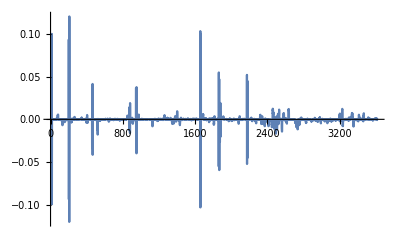

```mathematica
ListLinePlot[rsAlcxWeth, PlotRange->All]
```

```mathematica
edistAlcxWeth = EstimatedDistribution[rsAlcxWeth, StableDistribution[1, aAW, bAW, locAW, scaleAW]]
```

StableDistribution[1,0.838474,-0.181726,0.00011192,0.000231752]

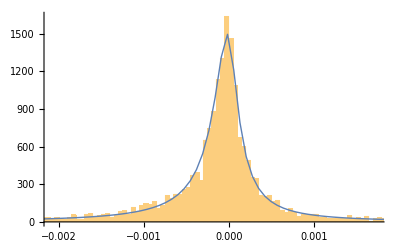

```mathematica
Show[Histogram[rsAlcxWeth, {0.00005}, "PDF"], Plot[PDF[edistAlcxWeth, x], {x, Min[rsAlcxWeth], Max[rsAlcxWeth]}, PlotRange->All, PlotStyle->Thick]]
```

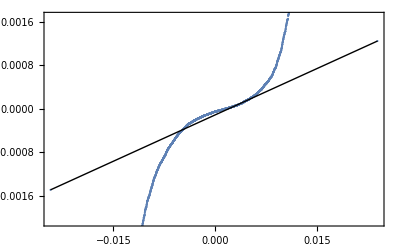

```mathematica
QuantilePlot[rsAlcxWeth]
```

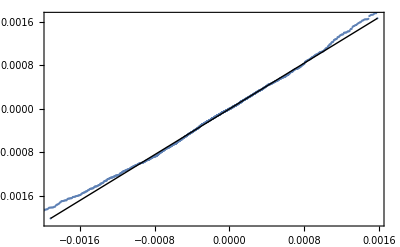

```mathematica
QuantilePlot[rsAlcxWeth, edistAlcxWeth]
```

```mathematica
(* That's scary. This is literally fuhgetaboutdit territory => Caps on payoff obviously very necessary ... *)
```

```mathematica
(* And just to go through them all, look at UNI/WETH ... How bad? *)
```

```mathematica
tblUniWeth = Import["30/data-1624665179_uni_weth-twap.csv"]
```

{{,timestamp,twap},{0,1.62208×10^9,1.01055×10^16},{1,1.62208×10^9,1.01007×10^16},{2,1.62208×10^9,1.00728×10^16},{3,1.62208×10^9,1.00671×10^16},{4,1.62208×10^9,1.00592×10^16},2320,{2325,1.62465×10^9,8.78565×10^15},{2326,1.62465×10^9,8.78524×10^15},{2327,1.62466×10^9,8.78139×10^15},{2328,1.62466×10^9,8.77619×10^15},{2329,1.62466×10^9,8.77331×10^15},{2330,1.62466×10^9,8.77378×10^15}}
 |  |  |  |

```mathematica
twapsUniWeth = Table[tblUniWeth[[i]][[3]], {i, 2, Length[tblUniWeth]}]
```

{1.01055×10^16,1.01007×10^16,1.00728×10^16,1.00671×10^16,1.00592×10^16,1.00392×10^16,1.00078×10^16,9.9933×10^15,9.99008×10^15,9.98171×10^15,9.96979×10^15,9.97023×10^15,9.95762×10^15,9.94493×10^15,9.93627×10^15,9.9233×10^15,9.92102×10^15,9.91161×10^15,9.91024×10^15,9.91762×10^15,9.94087×10^15,9.95482×10^15,9.9791×10^15,9.99584×10^15,1.00154×10^16,1.00343×10^16,1.00512×10^16,1.0072×10^16,1.00763×10^16,1.00755×10^16,1.00733×10^16,1.00751×10^16,1.00778×10^16,1.00874×10^16,1.00979×10^16,1.01099×10^16,1.01203×10^16,1.01438×10^16,1.01756×10^16,1.02191×10^16,1.02613×10^16,1.02839×10^16,1.03232×10^16,1.0341×10^16,1.03499×10^16,1.03509×10^16,1.03489×10^16,1.03328×10^16,1.03241×10^16,1.03251×10^16,1.03204×10^16,1.03085×10^16,1.02995×10^16,1.02972×10^16,1.02871×10^16,1.02856×10^16,1.02903×10^16,1.02943×10^16,1.02993×10^16,1.03189×10^16,1.03547×10^16,1.03636×10^16,1.03786×10^16,1.03933×10^16,1.04138×10^16,1.04354×10^16,1.04479×10^16,1.04773×10^16,1.04989×10^16,1.04978×10^16,1.04858×10^16,1.04781×10^16,1.0459×10^16,1.04418×10^16,1.04447×10^16,1.04533×10^16,1.04612×10^16,1.04725×10^16,1.04689×10^16,1.04676×10^16,1.04596×10^16,1.04446×10^16,1.04093×10^16,1.03827×10^16,1.03646×10^16,1.03545×10^16,1.03459×10^16,1.03374×10^16,1.03318×10^16,1.03124×10^16,1.03088×10^16,1.0313×10^16,1.03272×10^16,1.03446×10^16,1.03742×10^16,1.0385×10^16,1.03959×10^16,1.03988×10^16,1.03876×10^16,1.03787×10^16,1.03703×10^16,1.03712×10^16,1.03692×10^16,1.0374×10^16,1.03955×10^16,1.04133×10^16,1.0409×10^16,1.04055×10^16,1.039×10^16,1.03804×10^16,1.03786×10^16,1.03867×10^16,1.04066×10^16,1.04422×10^16,1.04623×10^16,1.0526×10^16,1.05542×10^16,1.05946×10^16,1.06452×10^16,1.0663×10^16,1.06977×10^16,1.07025×10^16,1.06907×10^16,1.06544×10^16,1.06203×10^16,1.05455×10^16,1.04964×10^16,1.04763×10^16,1.04626×10^16,1.0454×10^16,1.04437×10^16,1.04297×10^16,1.04147×10^16,1.03799×10^16,1.0355×10^16,1.03372×10^16,1.0333×10^16,1.03348×10^16,1.03426×10^16,1.03562×10^16,1.03766×10^16,1.03891×10^16,1.03966×10^16,1.04073×10^16,1.04154×10^16,1.04174×10^16,1.04167×10^16,1.04072×10^16,1.03797×10^16,1.03586×10^16,1.03403×10^16,1.03788×10^16,1.03896×10^16,1.0425×10^16,1.04351×10^16,1.04382×10^16,1.04338×10^16,1.04284×10^16,1.04194×10^16,1.04042×10^16,1.03916×10^16,1.03616×10^16,1.03506×10^16,1.0355×10^16,1.03559×10^16,1.0397×10^16,1.04527×10^16,1.03401×10^16,1.05552×10^16,1.0582×10^16,1.06399×10^16,1.06697×10^16,1.08388×10^16,1.07131×10^16,1.0723×10^16,1.07375×10^16,1.07419×10^16,1.07532×10^16,1.07818×10^16,1.08111×10^16,1.08398×10^16,1.08411×10^16,1.08563×10^16,1.08642×10^16,1.08679×10^16,1.08594×10^16,1.08559×10^16,1.08358×10^16,1.08101×10^16,1.08053×10^16,1.08015×10^16,1.08069×10^16,1.0809×10^16,1.08144×10^16,1.0798×10^16,1.07878×10^16,1.07462×10^16,1.07166×10^16,1.07005×10^16,1.06964×10^16,1.06939×10^16,1.06947×10^16,1.07007×10^16,1.06944×10^16,1.06831×10^16,1.06799×10^16,1.06752×10^16,1.06711×10^16,1.06794×10^16,1.06901×10^16,1.07112×10^16,1.07259×10^16,1.07371×10^16,1.07399×10^16,1.07388×10^16,1.07359×10^16,1.0728×10^16,1.0718×10^16,1.0701×10^16,1.06938×10^16,1.06934×10^16,1.06957×10^16,1.06927×10^16,1.0689×10^16,1.06815×10^16,1.06832×10^16,1.06835×10^16,1.0682×10^16,1.06754×10^16,1.06501×10^16,1.06358×10^16,1.06299×10^16,1.06391×10^16,1.06594×10^16,1.06908×10^16,1.07303×10^16,1.07445×10^16,1.07453×10^16,1.07383×10^16,1.07136×10^16,1.07013×10^16,1.06942×10^16,1.06857×10^16,1.0653×10^16,1.06341×10^16,1.06194×10^16,1.06072×10^16,1.0595×10^16,1.05963×10^16,1.05957×10^16,1.05887×10^16,1.05904×10^16,1.06012×10^16,1.05994×10^16,1.05985×10^16,1.06063×10^16,1.05922×10^16,1.05771×10^16,1.05482×10^16,1.05384×10^16,1.05071×10^16,1.04587×10^16,1.04006×10^16,1.03292×10^16,1.02916×10^16,1.02239×10^16,1.01795×10^16,1.01592×10^16,1.01529×10^16,1.01424×10^16,1.01071×10^16,1.01052×10^16,1.01035×10^16,1.01079×10^16,1.00869×10^16,1.00766×10^16,1.00686×10^16,1.00466×10^16,1.00295×10^16,1.00163×10^16,9.9986×10^15,9.97978×10^15,9.95792×10^15,9.91415×10^15,9.90958×10^15,9.9074×10^15,9.9078×10^15,9.90334×10^15,9.89406×10^15,9.89614×10^15,9.89464×10^15,9.90024×10^15,9.91026×10^15,9.94063×10^15,9.95062×10^15,9.96089×10^15,9.97326×10^15,9.98683×10^15,9.98894×10^15,9.99567×10^15,1.00326×10^16,1.00419×10^16,1.00514×10^16,1.00607×10^16,1.00693×10^16,1.00766×10^16,1.00853×10^16,1.00996×10^16,1.01057×10^16,1.00976×10^16,1.00746×10^16,1.00427×10^16,1.00108×10^16,9.98001×10^15,9.97206×10^15,9.9632×10^15,9.96505×10^15,9.9752×10^15,9.98603×10^15,9.99502×10^15,1.00129×10^16,1.00424×10^16,1.00696×10^16,1.00795×10^16,1.008×10^16,1.00831×10^16,1.00911×10^16,1.01023×10^16,1.0127×10^16,1.01502×10^16,1.01729×10^16,1.0197×10^16,1.02222×10^16,1.02788×10^16,1.0337×10^16,1.03592×10^16,1.0358×10^16,1.03428×10^16,1.03405×10^16,1.03376×10^16,1.03271×10^16,1.03249×10^16,1.03324×10^16,1.03244×10^16,1.03103×10^16,1.03028×10^16,1.03025×10^16,1.03071×10^16,1.0314×10^16,1.03293×10^16,1.03324×10^16,1.03564×10^16,9.27572×10^15,1.03432×10^16,1.03361×10^16,1.03567×10^16,1.03563×10^16,1.12319×10^16,1.03661×10^16,1.03643×10^16,1.03545×10^16,1.03512×10^16,1.03359×10^16,1.03186×10^16,1.03134×10^16,1.03067×10^16,1.03092×10^16,1.03285×10^16,1.03707×10^16,1.03826×10^16,1.03933×10^16,1.04065×10^16,1.04184×10^16,1.04514×10^16,1.04686×10^16,1.04816×10^16,1.04945×10^16,1.05043×10^16,1.05212×10^16,1.05501×10^16,1.05767×10^16,1.06047×10^16,1.06205×10^16,1.06524×10^16,1.06776×10^16,1.0715×10^16,1.07388×10^16,1.07605×10^16,1.07792×10^16,1.07821×10^16,1.07856×10^16,1.07913×10^16,1.08101×10^16,1.08218×10^16,1.08196×10^16,1.08206×10^16,1.08142×10^16,1.0795×10^16,1.07774×10^16,1.07734×10^16,1.07685×10^16,1.07696×10^16,1.07659×10^16,1.0763×10^16,1.076×10^16,1.07613×10^16,1.07354×10^16,1.07204×10^16,1.0692×10^16,1.0656×10^16,1.06051×10^16,1.06589×10^16,1.05292×10^16,1.04865×10^16,1.04577×10^16,1.04223×10^16,1.02639×10^16,1.03849×10^16,1.03845×10^16,1.03894×10^16,1.03868×10^16,1.03761×10^16,1.03097×10^16,1.03036×10^16,1.03097×10^16,1.03075×10^16,1.03033×10^16,1.03524×10^16,1.03526×10^16,1.03509×10^16,1.03611×10^16,1.03617×10^16,1.03871×10^16,1.0388×10^16,1.03901×10^16,1.0392×10^16,1.03933×10^16,1.04538×10^16,1.04471×10^16,1.04386×10^16,1.04419×10^16,1.04502×10^16,1.04477×10^16,1.04532×10^16,1.04624×10^16,1.0457×10^16,1.04481×10^16,1.04522×10^16,1.0456×10^16,1.04512×10^16,1.04435×10^16,1.04204×10^16,1.04054×10^16,1.03931×10^16,1.03758×10^16,1.03645×10^16,1.03636×10^16,1.03495×10^16,1.03416×10^16,1.03312×10^16,1.03257×10^16,1.03198×10^16,1.03109×10^16,1.03035×10^16,1.03029×10^16,1.03119×10^16,1.03224×10^16,1.0337×10^16,1.03579×10^16,1.03732×10^16,1.03881×10^16,1.04037×10^16,1.041×10^16,1.04198×10^16,1.04354×10^16,1.04384×10^16,1.04461×10^16,1.04491×10^16,1.04518×10^16,1.04546×10^16,1.0456×10^16,1.04561×10^16,1.04536×10^16,1.04372×10^16,1.04286×10^16,1.04054×10^16,1.03985×10^16,1.03969×10^16,1.03941×10^16,1.03839×10^16,1.03764×10^16,1.03736×10^16,1.03581×10^16,1.03443×10^16,1.03309×10^16,1.03191×10^16,1.03203×10^16,1.03243×10^16,1.03371×10^16,1.03767×10^16,1.0389×10^16,1.04051×10^16,1.04169×10^16,1.0451×10^16,1.04556×10^16,1.04644×10^16,1.04777×10^16,1.04754×10^16,1.04645×10^16,1.04554×10^16,1.04493×10^16,1.04509×10^16,1.04498×10^16,1.04344×10^16,1.04328×10^16,1.04236×10^16,1.03889×10^16,1.03689×10^16,1.03569×10^16,1.03386×10^16,1.03282×10^16,1.03081×10^16,1.02963×10^16,1.02921×10^16,1.02938×10^16,1.02907×10^16,1.02938×10^16,1.02991×10^16,1.03044×10^16,1.03107×10^16,1.0331×10^16,1.03443×10^16,1.0348×10^16,1.03621×10^16,1.03629×10^16,1.03595×10^16,1.03611×10^16,1.03616×10^16,1.03846×10^16,1.03904×10^16,1.03948×10^16,1.03984×10^16,1.03873×10^16,1.03789×10^16,1.03699×10^16,1.03687×10^16,1.03677×10^16,1.03664×10^16,1.03652×10^16,1.03654×10^16,1.03645×10^16,1.03559×10^16,1.03518×10^16,1.03295×10^16,1.03233×10^16,1.03185×10^16,1.03204×10^16,1.03108×10^16,1.03079×10^16,1.0299×10^16,1.02792×10^16,1.02586×10^16,1.02216×10^16,1.02035×10^16,1.01933×10^16,1.01805×10^16,1.01793×10^16,1.01764×10^16,1.01844×10^16,1.0191×10^16,1.02156×10^16,1.02285×10^16,1.0239×10^16,1.02534×10^16,1.02568×10^16,1.02508×10^16,1.02486×10^16,1.02418×10^16,1.02343×10^16,1.02343×10^16,1.02366×10^16,1.02393×10^16,1.02511×10^16,1.02635×10^16,1.02649×10^16,1.02664×10^16,1.02661×10^16,1.02578×10^16,1.0246×10^16,1.02444×10^16,1.02378×10^16,1.02258×10^16,1.02128×10^16,1.02006×10^16,1.01747×10^16,1.01634×10^16,1.01588×10^16,1.01718×10^16,1.01807×10^16,1.0192×10^16,1.01976×10^16,1.02×10^16,1.02141×10^16,1.02153×10^16,1.02089×10^16,1.02036×10^16,1.01967×10^16,1.01845×10^16,1.01746×10^16,1.01629×10^16,1.01629×10^16,1.01518×10^16,1.01473×10^16,1.0135×10^16,1.01286×10^16,1.01205×10^16,1.01187×10^16,1.01147×10^16,1.01201×10^16,1.01347×10^16,1.01383×10^16,1.014×10^16,1.01452×10^16,1.01499×10^16,1.01488×10^16,1.01562×10^16,1.01581×10^16,1.01634×10^16,1.01597×10^16,1.01569×10^16,1.01392×10^16,1.01242×10^16,1.0113×10^16,1.01×10^16,1.0111×10^16,1.01145×10^16,1.01138×10^16,1.01116×10^16,1.01086×10^16,1.00971×10^16,1.01022×10^16,1.01144×10^16,1.01316×10^16,1.01385×10^16,1.01313×10^16,1.01359×10^16,1.01371×10^16,1.01354×10^16,1.01448×10^16,1.01659×10^16,1.0157×10^16,1.01455×10^16,1.0138×10^16,1.01083×10^16,1.00973×10^16,1.00864×10^16,1.00727×10^16,1.00692×10^16,1.0058×10^16,1.00408×10^16,1.00321×10^16,1.00331×10^16,1.00342×10^16,1.00515×10^16,1.00778×10^16,1.00804×10^16,1.00928×10^16,1.00939×10^16,1.00906×10^16,1.00876×10^16,1.00863×10^16,1.00503×10^16,1.00373×10^16,1.00321×10^16,1.00271×10^16,1.00224×10^16,1.00235×10^16,1.00284×10^16,1.00319×10^16,1.00331×10^16,1.00357×10^16,1.00285×10^16,1.00094×10^16,9.99433×10^15,9.98227×10^15,9.9728×10^15,9.96418×10^15,9.94256×10^15,9.95434×10^15,9.96902×10^15,9.9791×10^15,9.99438×10^15,9.98884×10^15,9.982×10^15,9.97086×10^15,9.95526×10^15,9.94937×10^15,9.95601×10^15,9.9591×10^15,9.95464×10^15,9.94775×10^15,9.93679×10^15,9.9163×10^15,9.90624×10^15,9.89896×10^15,9.89075×10^15,9.88664×10^15,9.88296×10^15,9.86653×10^15,9.86681×10^15,9.86048×10^15,9.85721×10^15,9.85768×10^15,9.8694×10^15,9.87508×10^15,9.88682×10^15,9.88745×10^15,9.89557×10^15,9.89955×10^15,9.90251×10^15,9.90949×10^15,9.91453×10^15,9.90646×10^15,9.89361×10^15,9.88485×10^15,9.86476×10^15,9.84741×10^15,9.86033×10^15,9.86375×10^15,9.86691×10^15,9.86561×10^15,9.85804×10^15,9.84128×10^15,9.84211×10^15,9.84522×10^15,9.84863×10^15,9.84567×10^15,9.84572×10^15,9.84117×10^15,9.83074×10^15,9.82881×10^15,9.83481×10^15,9.84441×10^15,9.85397×10^15,9.85841×10^15,9.85828×10^15,9.8618×10^15,9.86747×10^15,9.89991×10^15,9.91347×10^15,9.92241×10^15,9.9164×10^15,9.91029×10^15,9.88718×10^15,9.87468×10^15,9.86925×10^15,9.86372×10^15,9.85481×10^15,9.84876×10^15,9.85292×10^15,9.85507×10^15,9.85751×10^15,9.86139×10^15,9.86116×10^15,9.84336×10^15,9.8437×10^15,9.84469×10^15,9.84832×10^15,9.84758×10^15,9.85004×10^15,9.82487×10^15,9.81427×10^15,9.80491×10^15,9.79739×10^15,9.8014×10^15,9.81399×10^15,9.81713×10^15,9.82384×10^15,9.82857×10^15,9.8334×10^15,9.83106×10^15,9.82887×10^15,9.82773×10^15,9.82274×10^15,9.81887×10^15,9.81868×10^15,9.81842×10^15,9.81844×10^15,9.81917×10^15,9.81907×10^15,9.81872×10^15,9.81421×10^15,9.81517×10^15,9.81619×10^15,9.81248×10^15,9.8068×10^15,9.80344×10^15,9.79695×10^15,9.78304×10^15,9.77846×10^15,9.77834×10^15,9.77607×10^15,9.77384×10^15,9.77569×10^15,9.78286×10^15,9.79108×10^15,9.80207×10^15,9.80274×10^15,9.81069×10^15,9.8128×10^15,9.80786×10^15,9.7922×10^15,9.77812×10^15,9.76965×10^15,9.75851×10^15,9.75495×10^15,9.75011×10^15,9.73953×10^15,9.71935×10^15,9.70099×10^15,9.69804×10^15,9.69435×10^15,9.69582×10^15,9.70259×10^15,9.71368×10^15,9.71876×10^15,9.72847×10^15,9.73709×10^15,9.7546×10^15,9.76963×10^15,9.77635×10^15,9.78142×10^15,9.79031×10^15,9.80354×10^15,9.82344×10^15,9.84043×10^15,9.8394×10^15,9.83841×10^15,9.83009×10^15,9.82004×10^15,9.80759×10^15,9.79943×10^15,9.78521×10^15,9.76989×10^15,9.76876×10^15,9.76698×10^15,9.76575×10^15,9.76594×10^15,9.76481×10^15,9.75503×10^15,9.74985×10^15,9.74197×10^15,9.73757×10^15,9.73034×10^15,9.72349×10^15,9.71841×10^15,9.71848×10^15,9.73235×10^15,9.74199×10^15,9.7524×10^15,9.75531×10^15,9.74227×10^15,9.73055×10^15,9.72353×10^15,9.71185×10^15,9.70911×10^15,9.69772×10^15,9.68955×10^15,9.66469×10^15,9.63085×10^15,9.61126×10^15,9.59549×10^15,9.58338×10^15,9.57478×10^15,9.56147×10^15,9.54724×10^15,9.53428×10^15,9.52851×10^15,9.52577×10^15,9.5228×10^15,9.52357×10^15,9.52646×10^15,9.52886×10^15,9.53481×10^15,9.54809×10^15,9.55012×10^15,9.55885×10^15,9.56406×10^15,9.56339×10^15,9.56108×10^15,9.55646×10^15,9.54898×10^15,9.5491×10^15,9.55401×10^15,9.55471×10^15,9.55702×10^15,9.56233×10^15,9.5615×10^15,9.55986×10^15,9.55858×10^15,9.55822×10^15,9.55222×10^15,9.55035×10^15,9.54718×10^15,9.54543×10^15,9.55236×10^15,9.55765×10^15,9.57054×10^15,9.58185×10^15,9.58028×10^15,9.56755×10^15,9.56379×10^15,9.55623×10^15,9.54634×10^15,9.54298×10^15,9.53422×10^15,9.53063×10^15,9.52507×10^15,9.51972×10^15,9.51276×10^15,9.50869×10^15,9.49991×10^15,9.49907×10^15,9.49412×10^15,9.4918×10^15,9.49011×10^15,9.50104×10^15,9.51432×10^15,9.53642×10^15,9.54423×10^15,9.55244×10^15,9.54397×10^15,9.53592×10^15,9.53154×10^15,9.5242×10^15,9.52048×10^15,9.51825×10^15,9.51662×10^15,9.51728×10^15,9.51367×10^15,9.50752×10^15,9.50327×10^15,9.4915×10^15,9.48675×10^15,9.47576×10^15,9.46552×10^15,9.46303×10^15,9.44654×10^15,9.44318×10^15,9.45274×10^15,9.47696×10^15,9.48229×10^15,9.51677×10^15,9.56033×10^15,9.58594×10^15,9.60053×10^15,9.60624×10^15,9.62024×10^15,9.62833×10^15,9.6305×10^15,9.63108×10^15,9.63225×10^15,9.63665×10^15,9.64056×10^15,9.64192×10^15,9.64745×10^15,9.64817×10^15,9.64456×10^15,9.64156×10^15,9.6399×10^15,9.63929×10^15,9.63906×10^15,9.64061×10^15,9.64757×10^15,9.6594×10^15,9.66593×10^15,9.66891×10^15,9.66928×10^15,9.67075×10^15,9.66278×10^15,9.65003×10^15,9.61828×10^15,9.60642×10^15,9.59209×10^15,9.57803×10^15,9.57243×10^15,9.54462×10^15,9.49919×10^15,9.47563×10^15,9.44997×10^15,9.44383×10^15,9.41723×10^15,9.41022×10^15,9.38365×10^15,9.37146×10^15,9.36312×10^15,9.34689×10^15,9.3345×10^15,9.32371×10^15,9.33535×10^15,9.34913×10^15,9.34781×10^15,9.35802×10^15,9.3401×10^15,9.32571×10^15,9.31273×10^15,9.30973×10^15,9.31026×10^15,9.30705×10^15,9.3026×10^15,9.29147×10^15,9.29733×10^15,9.29739×10^15,9.29863×10^15,9.30341×10^15,9.30949×10^15,9.30997×10^15,9.3159×10^15,9.31585×10^15,9.31265×10^15,9.31304×10^15,9.31619×10^15,9.31899×10^15,9.32505×10^15,9.33073×10^15,9.32817×10^15,9.32545×10^15,9.31707×10^15,9.30981×10^15,9.30185×10^15,9.30021×10^15,9.29403×10^15,9.28928×10^15,9.28229×10^15,9.26461×10^15,9.25504×10^15,9.24335×10^15,9.24129×10^15,9.24116×10^15,9.2335×10^15,9.22615×10^15,9.19572×10^15,9.15912×10^15,9.097×10^15,9.07823×10^15,9.08571×10^15,9.09227×10^15,9.10349×10^15,9.133×10^15,9.14034×10^15,9.14584×10^15,9.15127×10^15,9.15043×10^15,9.15251×10^15,9.16357×10^15,9.17534×10^15,9.18697×10^15,9.19743×10^15,9.2074×10^15,9.21704×10^15,9.23099×10^15,9.25679×10^15,9.28074×10^15,9.28804×10^15,9.29266×10^15,9.30206×10^15,9.31946×10^15,9.33041×10^15,9.33901×10^15,9.33623×10^15,9.33627×10^15,9.33412×10^15,9.33198×10^15,9.32776×10^15,9.33038×10^15,9.32923×10^15,9.32707×10^15,9.3175×10^15,9.31027×10^15,9.29215×10^15,9.2539×10^15,9.22683×10^15,9.21123×10^15,9.21029×10^15,9.2201×10^15,9.23071×10^15,9.24195×10^15,9.24602×10^15,9.2509×10^15,9.24806×10^15,9.25006×10^15,9.26563×10^15,9.27238×10^15,9.28134×10^15,9.29126×10^15,9.30229×10^15,9.33171×10^15,9.34138×10^15,9.36258×10^15,9.39159×10^15,9.40431×10^15,9.39977×10^15,9.39469×10^15,9.37626×10^15,9.35899×10^15,9.35169×10^15,9.34874×10^15,9.34592×10^15,9.34472×10^15,9.35609×10^15,9.38201×10^15,9.40093×10^15,9.41645×10^15,9.43093×10^15,9.48861×10^15,9.48482×10^15,9.47546×10^15,9.47355×10^15,9.47211×10^15,9.47629×10^15,9.48142×10^15,9.48646×10^15,9.4915×10^15,9.50759×10^15,9.50614×10^15,9.50484×10^15,9.5081×10^15,9.51996×10^15,9.50586×10^15,9.50354×10^15,9.50095×10^15,9.49875×10^15,9.49316×10^15,9.4882×10^15,9.47961×10^15,9.46285×10^15,9.45683×10^15,9.45256×10^15,9.45058×10^15,9.44783×10^15,9.44932×10^15,9.44905×10^15,9.44728×10^15,9.44771×10^15,9.45469×10^15,9.45947×10^15,9.46957×10^15,9.48002×10^15,9.51256×10^15,9.55899×10^15,9.59917×10^15,9.61317×10^15,9.61735×10^15,9.62192×10^15,9.62164×10^15,9.62147×10^15,9.62202×10^15,9.62351×10^15,9.63855×10^15,9.64757×10^15,9.64913×10^15,9.64407×10^15,9.63824×10^15,9.62684×10^15,9.6165×10^15,9.60739×10^15,9.58952×10^15,9.58906×10^15,9.58195×10^15,9.57688×10^15,9.57263×10^15,9.57404×10^15,9.57441×10^15,9.57414×10^15,9.5714×10^15,9.56461×10^15,9.56116×10^15,9.5623×10^15,9.56306×10^15,9.56638×10^15,9.57173×10^15,9.57633×10^15,9.57292×10^15,9.56627×10^15,9.56026×10^15,9.54914×10^15,9.55357×10^15,9.55222×10^15,9.55644×10^15,9.5598×10^15,9.57258×10^15,9.57362×10^15,9.57534×10^15,9.57987×10^15,9.57956×10^15,9.57718×10^15,9.5768×10^15,9.5756×10^15,9.57434×10^15,9.57339×10^15,9.57262×10^15,9.57148×10^15,9.57018×10^15,9.56936×10^15,9.56797×10^15,9.56713×10^15,9.56405×10^15,9.56176×10^15,9.55669×10^15,9.55234×10^15,9.55073×10^15,9.54776×10^15,9.54734×10^15,9.54694×10^15,9.54682×10^15,9.5464×10^15,9.54635×10^15,9.54959×10^15,9.55036×10^15,9.55064×10^15,9.55087×10^15,9.55444×10^15,9.55241×10^15,9.55486×10^15,9.55986×10^15,9.5454×10^15,9.53613×10^15,9.53313×10^15,9.52375×10^15,9.52156×10^15,9.52184×10^15,9.52381×10^15,9.52443×10^15,9.52525×10^15,9.52631×10^15,9.52624×10^15,9.526×10^15,9.52575×10^15,9.52555×10^15,9.52422×10^15,9.52059×10^15,9.5121×10^15,9.50353×10^15,9.49515×10^15,9.49208×10^15,9.49166×10^15,9.49547×10^15,9.49639×10^15,9.48513×10^15,9.46314×10^15,9.4319×10^15,9.4128×10^15,9.41004×10^15,9.40422×10^15,9.40128×10^15,9.39309×10^15,9.3916×10^15,9.38927×10^15,9.38949×10^15,9.38991×10^15,9.39034×10^15,9.38743×10^15,9.37167×10^15,9.36874×10^15,9.35755×10^15,9.34323×10^15,9.33004×10^15,9.31735×10^15,9.31389×10^15,9.31338×10^15,9.31262×10^15,9.31164×10^15,9.30809×10^15,9.3067×10^15,9.30556×10^15,9.30573×10^15,9.30529×10^15,9.30299×10^15,9.30068×10^15,9.29826×10^15,9.29735×10^15,9.3013×10^15,9.32331×10^15,9.33273×10^15,9.34868×10^15,9.35401×10^15,9.34292×10^15,9.33486×10^15,9.3233×10^15,9.31112×10^15,9.28493×10^15,9.28408×10^15,9.28407×10^15,9.28176×10^15,9.27021×10^15,9.266×10^15,9.26369×10^15,9.26122×10^15,9.26173×10^15,9.26021×10^15,9.25066×10^15,9.24295×10^15,9.20764×10^15,9.20588×10^15,9.20573×10^15,9.20883×10^15,9.21748×10^15,9.23036×10^15,9.25644×10^15,9.2759×10^15,9.28672×10^15,9.29172×10^15,9.28864×10^15,9.27421×10^15,9.265×10^15,9.2492×10^15,9.24215×10^15,9.23283×10^15,9.22109×10^15,9.18238×10^15,9.16667×10^15,9.14891×10^15,9.13782×10^15,9.12947×10^15,9.11373×10^15,9.10975×10^15,9.09639×10^15,9.08403×10^15,9.06562×10^15,9.05708×10^15,9.04753×10^15,9.03795×10^15,9.02984×10^15,9.01868×10^15,9.00838×10^15,8.98561×10^15,8.96104×10^15,8.93493×10^15,8.89945×10^15,8.90018×10^15,8.90584×10^15,8.91259×10^15,8.92101×10^15,8.92122×10^15,8.91928×10^15,8.915×10^15,8.9129×10^15,8.90803×10^15,8.9075×10^15,8.89384×10^15,8.89032×10^15,8.8813×10^15,8.87675×10^15,8.87782×10^15,8.90323×10^15,8.90823×10^15,8.91721×10^15,8.92053×10^15,8.9211×10^15,8.9149×10^15,8.91528×10^15,8.91284×10^15,8.92044×10^15,8.91823×10^15,8.91528×10^15,8.91269×10^15,8.91492×10^15,8.91307×10^15,8.91241×10^15,8.91392×10^15,8.91561×10^15,8.91715×10^15,8.93012×10^15,8.96305×10^15,8.97177×10^15,8.97735×10^15,8.98431×10^15,8.99137×10^15,9.00225×10^15,9.00118×10^15,8.9993×10^15,8.99762×10^15,8.98735×10^15,8.98442×10^15,8.98683×10^15,8.98887×10^15,8.98894×10^15,9.01128×10^15,9.01309×10^15,9.00515×10^15,9.00838×10^15,9.00622×10^15,9.00222×10^15,9.00488×10^15,9.00894×10^15,9.00683×10^15,9.00709×10^15,9.00469×10^15,9.00148×10^15,9.00133×10^15,9.00043×10^15,8.9994×10^15,8.99591×10^15,8.99509×10^15,8.99295×10^15,8.99179×10^15,8.99205×10^15,8.99217×10^15,8.99205×10^15,8.99192×10^15,8.99168×10^15,8.98758×10^15,8.98524×10^15,8.97481×10^15,8.96562×10^15,8.96101×10^15,8.94826×10^15,8.94082×10^15,8.92271×10^15,8.92272×10^15,8.92244×10^15,8.91958×10^15,8.9173×10^15,8.90815×10^15,8.90041×10^15,8.89744×10^15,8.88363×10^15,8.88017×10^15,8.87564×10^15,8.87666×10^15,8.87608×10^15,8.87304×10^15,8.8668×10^15,8.86429×10^15,8.85963×10^15,8.85116×10^15,8.84572×10^15,8.83777×10^15,8.83079×10^15,8.82848×10^15,8.8256×10^15,8.82647×10^15,8.82827×10^15,8.83232×10^15,8.82965×10^15,8.82695×10^15,8.82144×10^15,8.8169×10^15,8.81139×10^15,8.80843×10^15,8.80852×10^15,8.80862×10^15,8.80856×10^15,8.80756×10^15,8.80827×10^15,8.82294×10^15,8.82926×10^15,8.84415×10^15,8.88164×10^15,8.91339×10^15,8.94117×10^15,8.94987×10^15,8.9704×10^15,8.98095×10^15,8.9874×10^15,8.99651×10^15,9.00128×10^15,9.01142×10^15,9.02026×10^15,9.02213×10^15,9.03149×10^15,9.0369×10^15,9.04108×10^15,9.0467×10^15,9.05461×10^15,9.0729×10^15,9.10766×10^15,9.1233×10^15,9.19203×10^15,9.21301×10^15,9.25094×10^15,9.25134×10^15,9.25233×10^15,9.25647×10^15,9.25849×10^15,9.26607×10^15,9.27188×10^15,9.27414×10^15,9.26977×10^15,9.26609×10^15,9.25955×10^15,9.25818×10^15,9.25602×10^15,9.25996×10^15,9.25273×10^15,9.24664×10^15,9.24164×10^15,9.23092×10^15,9.21782×10^15,9.20052×10^15,9.19179×10^15,9.18889×10^15,9.18823×10^15,9.18498×10^15,9.18976×10^15,9.19162×10^15,9.19474×10^15,9.20199×10^15,9.206×10^15,9.21157×10^15,9.21994×10^15,9.21485×10^15,1.04388×10^16,9.20047×10^15,9.19303×10^15,9.19025×10^15,9.18673×10^15,7.96762×10^15,9.17613×10^15,9.16721×10^15,9.16322×10^15,9.16279×10^15,9.15931×10^15,9.15683×10^15,9.1611×10^15,9.16156×10^15,9.16262×10^15,9.16567×10^15,9.16676×10^15,9.16793×10^15,9.17207×10^15,9.21761×10^15,9.25546×10^15,9.26819×10^15,9.26938×10^15,9.27943×10^15,9.27538×10^15,9.27175×10^15,9.27484×10^15,9.28177×10^15,9.2697×10^15,9.26184×10^15,9.25869×10^15,9.25217×10^15,9.2552×10^15,9.28037×10^15,9.29957×10^15,9.31223×10^15,9.31483×10^15,9.31896×10^15,9.31347×10^15,9.31283×10^15,9.31205×10^15,9.30789×10^15,9.30227×10^15,9.29881×10^15,9.2889×10^15,9.28261×10^15,9.28268×10^15,9.28277×10^15,9.28284×10^15,9.28326×10^15,9.2835×10^15,9.27704×10^15,9.27516×10^15,9.28477×10^15,9.28645×10^15,9.2937×10^15,9.32256×10^15,9.33082×10^15,9.34625×10^15,9.34943×10^15,9.35034×10^15,9.34589×10^15,9.34384×10^15,9.34364×10^15,9.34354×10^15,9.34089×10^15,9.33553×10^15,9.33342×10^15,9.33149×10^15,9.32955×10^15,9.33078×10^15,9.33133×10^15,9.33082×10^15,9.33072×10^15,9.33036×10^15,9.32491×10^15,9.31857×10^15,9.31574×10^15,9.31503×10^15,9.3137×10^15,9.3117×10^15,9.30633×10^15,9.30159×10^15,9.29586×10^15,9.29412×10^15,9.29153×10^15,9.28554×10^15,9.27986×10^15,9.2702×10^15,9.26568×10^15,9.26368×10^15,9.26441×10^15,9.2651×10^15,9.26653×10^15,9.26081×10^15,9.25618×10^15,9.25162×10^15,9.24654×10^15,9.23836×10^15,9.23817×10^15,9.23767×10^15,9.23745×10^15,9.23688×10^15,9.23099×10^15,9.2276×10^15,9.22133×10^15,9.21683×10^15,9.21511×10^15,9.21552×10^15,9.21772×10^15,9.22113×10^15,9.2242×10^15,9.22378×10^15,9.22371×10^15,9.2236×10^15,9.22432×10^15,9.22502×10^15,9.22615×10^15,9.22654×10^15,9.22403×10^15,9.2228×10^15,9.20814×10^15,9.18466×10^15,9.17714×10^15,9.16636×10^15,9.16566×10^15,9.16607×10^15,9.17005×10^15,9.17246×10^15,9.17668×10^15,9.17908×10^15,9.18289×10^15,9.18678×10^15,9.1996×10^15,9.20438×10^15,9.20807×10^15,9.2094×10^15,9.21008×10^15,9.21218×10^15,9.21388×10^15,9.21867×10^15,9.22536×10^15,9.22534×10^15,9.22504×10^15,9.22368×10^15,9.22207×10^15,9.21743×10^15,9.21208×10^15,9.20828×10^15,9.19116×10^15,9.14524×10^15,9.11933×10^15,9.10965×10^15,9.10562×10^15,9.10154×10^15,9.08962×10^15,9.0783×10^15,9.07432×10^15,9.07188×10^15,9.07275×10^15,9.07342×10^15,9.07777×10^15,9.08344×10^15,9.09752×10^15,9.10291×10^15,9.10438×10^15,9.10769×10^15,9.11164×10^15,9.11295×10^15,9.12113×10^15,9.13001×10^15,9.12956×10^15,9.12922×10^15,9.13354×10^15,9.14462×10^15,9.15375×10^15,9.16721×10^15,9.17447×10^15,9.17618×10^15,9.18357×10^15,9.18801×10^15,9.19429×10^15,9.19961×10^15,9.20658×10^15,9.22475×10^15,9.23541×10^15,9.25566×10^15,9.25959×10^15,9.26369×10^15,9.26648×10^15,9.26559×10^15,9.26484×10^15,9.27131×10^15,9.27409×10^15,9.28676×10^15,9.293×10^15,9.30092×10^15,9.30681×10^15,9.30785×10^15,9.30885×10^15,9.31044×10^15,9.31203×10^15,9.31412×10^15,9.3188×10^15,9.32126×10^15,9.31881×10^15,9.31646×10^15,9.31453×10^15,9.3132×10^15,9.31212×10^15,9.31003×10^15,9.30958×10^15,9.30786×10^15,9.30754×10^15,9.30732×10^15,9.30709×10^15,9.31×10^15,9.3128×10^15,9.32001×10^15,9.31197×10^15,9.30782×10^15,9.30386×10^15,9.30393×10^15,9.30311×10^15,9.30717×10^15,9.3099×10^15,9.31328×10^15,9.30999×10^15,9.29902×10^15,9.28705×10^15,9.28605×10^15,9.28574×10^15,9.28595×10^15,9.28516×10^15,9.28389×10^15,9.28462×10^15,9.28719×10^15,9.28959×10^15,9.29623×10^15,9.31234×10^15,9.31834×10^15,9.32352×10^15,9.32444×10^15,9.32433×10^15,9.32248×10^15,9.32013×10^15,9.30697×10^15,9.29384×10^15,9.28827×10^15,9.2819×10^15,9.27487×10^15,9.26567×10^15,9.25141×10^15,9.24987×10^15,9.24942×10^15,9.25035×10^15,9.25332×10^15,9.25864×10^15,9.26283×10^15,9.26686×10^15,9.27092×10^15,9.26388×10^15,9.26106×10^15,9.25964×10^15,9.25809×10^15,9.25693×10^15,9.26432×10^15,9.26655×10^15,9.2648×10^15,9.25827×10^15,9.25453×10^15,9.23481×10^15,9.23379×10^15,9.23195×10^15,9.23396×10^15,9.23558×10^15,9.23861×10^15,9.23752×10^15,9.22214×10^15,9.21×10^15,9.19555×10^15,9.17929×10^15,9.17204×10^15,9.16281×10^15,9.15565×10^15,9.15363×10^15,9.15344×10^15,9.15627×10^15,9.1594×10^15,9.16549×10^15,9.16308×10^15,9.16225×10^15,9.1615×10^15,9.16395×10^15,9.16001×10^15,9.15307×10^15,9.15107×10^15,9.14646×10^15,9.14316×10^15,9.14243×10^15,9.14246×10^15,9.13819×10^15,9.13698×10^15,9.13459×10^15,9.13378×10^15,9.13383×10^15,9.13637×10^15,9.13646×10^15,9.13999×10^15,9.14209×10^15,9.15082×10^15,9.16784×10^15,9.17122×10^15,9.17695×10^15,9.18019×10^15,9.18203×10^15,9.17644×10^15,9.17102×10^15,9.16774×10^15,9.16089×10^15,9.15524×10^15,9.15679×10^15,9.15775×10^15,9.16234×10^15,9.16548×10^15,9.17166×10^15,9.18377×10^15,9.18728×10^15,9.1932×10^15,9.1983×10^15,9.19741×10^15,9.1957×10^15,9.1948×10^15,9.19343×10^15,9.19566×10^15,9.19717×10^15,9.19824×10^15,9.20057×10^15,9.20816×10^15,9.21563×10^15,9.21642×10^15,9.2161×10^15,9.21735×10^15,9.21495×10^15,9.21034×10^15,9.20699×10^15,9.20378×10^15,9.19585×10^15,9.19186×10^15,9.19045×10^15,9.18783×10^15,9.1867×10^15,9.18498×10^15,9.18289×10^15,9.18288×10^15,9.18469×10^15,9.18823×10^15,9.19194×10^15,9.19145×10^15,9.19251×10^15,9.19188×10^15,9.18808×10^15,9.18459×10^15,9.18125×10^15,9.17633×10^15,9.17232×10^15,9.17117×10^15,9.17009×10^15,9.16917×10^15,9.16022×10^15,9.15978×10^15,9.15944×10^15,9.15607×10^15,9.14766×10^15,9.12867×10^15,9.1012×10^15,9.079×10^15,9.06556×10^15,9.06217×10^15,9.05861×10^15,9.05627×10^15,9.05319×10^15,9.04518×10^15,9.04425×10^15,9.0455×10^15,9.05047×10^15,9.05288×10^15,9.05848×10^15,9.06417×10^15,9.08365×10^15,9.11778×10^15,9.13082×10^15,9.13875×10^15,9.13935×10^15,9.14133×10^15,9.14207×10^15,9.14582×10^15,9.14851×10^15,9.15174×10^15,9.15584×10^15,9.15862×10^15,9.16227×10^15,9.16146×10^15,9.16075×10^15,9.15827×10^15,9.15446×10^15,9.14813×10^15,9.15709×10^15,9.17116×10^15,9.18834×10^15,9.19903×10^15,9.21505×10^15,9.21366×10^15,9.20275×10^15,9.17154×10^15,9.15408×10^15,9.14727×10^15,9.14031×10^15,9.13426×10^15,9.12571×10^15,9.12613×10^15,9.14182×10^15,9.15013×10^15,9.16161×10^15,9.17741×10^15,9.1823×10^15,9.18434×10^15,9.18998×10^15,9.19298×10^15,9.20339×10^15,9.20537×10^15,9.20333×10^15,9.20181×10^15,9.2025×10^15,9.20356×10^15,9.20595×10^15,9.21217×10^15,9.20746×10^15,9.20726×10^15,9.20602×10^15,9.20322×10^15,9.20455×10^15,9.21439×10^15,9.21714×10^15,9.21907×10^15,9.22869×10^15,9.23408×10^15,9.23586×10^15,9.2442×10^15,9.24916×10^15,9.25291×10^15,9.25889×10^15,9.25117×10^15,9.2477×10^15,9.24425×10^15,9.23576×10^15,9.22882×10^15,9.22074×10^15,9.21904×10^15,9.21713×10^15,9.22676×10^15,9.23191×10^15,9.23399×10^15,9.22775×10^15,9.22353×10^15,9.21682×10^15,9.20676×10^15,9.20167×10^15,9.1921×10^15,9.17968×10^15,9.1733×10^15,9.16092×10^15,9.1463×10^15,9.14935×10^15,9.1418×10^15,9.13959×10^15,9.13446×10^15,9.13167×10^15,9.1188×10^15,9.11842×10^15,9.1094×10^15,9.10109×10^15,9.0901×10^15,9.08702×10^15,9.07599×10^15,9.06657×10^15,9.03977×10^15,9.02297×10^15,9.00939×10^15,8.98535×10^15,8.97013×10^15,8.94271×10^15,8.91909×10^15,8.90071×10^15,8.86843×10^15,8.81492×10^15,8.81195×10^15,8.80927×10^15,8.81194×10^15,8.80758×10^15,8.80603×10^15,8.79982×10^15,8.78277×10^15,8.75093×10^15,8.72935×10^15,8.72826×10^15,8.72664×10^15,8.73173×10^15,8.74847×10^15,8.76014×10^15,8.76274×10^15,8.76308×10^15,8.76762×10^15,8.77466×10^15,8.76638×10^15,8.75655×10^15,8.75276×10^15,8.73393×10^15,8.68547×10^15,8.64748×10^15,8.61675×10^15,8.5737×10^15,8.48888×10^15,8.45747×10^15,8.44552×10^15,8.42758×10^15,8.41348×10^15,8.37983×10^15,8.36231×10^15,8.33382×10^15,8.2991×10^15,8.28873×10^15,8.29484×10^15,8.31609×10^15,8.33502×10^15,8.37118×10^15,8.43018×10^15,8.44674×10^15,8.46607×10^15,8.4799×10^15,8.50884×10^15,8.54613×10^15,8.55612×10^15,8.56043×10^15,8.5612×10^15,8.5588×10^15,8.54421×10^15,8.52789×10^15,8.51699×10^15,8.50294×10^15,8.48801×10^15,8.48467×10^15,8.48158×10^15,8.47576×10^15,8.47338×10^15,8.47427×10^15,8.46542×10^15,8.45588×10^15,8.4493×10^15,8.43701×10^15,8.41525×10^15,8.37874×10^15,8.32492×10^15,8.29159×10^15,8.26903×10^15,8.24261×10^15,8.22857×10^15,8.17154×10^15,8.15778×10^15,8.16039×10^15,8.17507×10^15,8.1963×10^15,8.22838×10^15,8.22382×10^15,8.21099×10^15,8.16655×10^15,8.07731×10^15,8.03588×10^15,7.94108×10^15,7.9451×10^15,7.99464×10^15,8.02402×10^15,8.10161×10^15,8.17354×10^15,8.21083×10^15,8.24324×10^15,8.27518×10^15,8.33115×10^15,8.41383×10^15,8.48533×10^15,8.5455×10^15,8.59724×10^15,8.63009×10^15,8.65289×10^15,8.67576×10^15,8.6964×10^15,8.71483×10^15,8.73664×10^15,8.74423×10^15,8.7481×10^15,8.74973×10^15,8.758×10^15,8.76419×10^15,8.77678×10^15,8.77834×10^15,8.76486×10^15,8.74792×10^15,8.74107×10^15,8.72057×10^15,8.72211×10^15,8.71542×10^15,8.71798×10^15,8.71266×10^15,8.71402×10^15,8.71406×10^15,8.77332×10^15,8.78044×10^15,8.8016×10^15,8.8305×10^15,8.84078×10^15,8.86664×10^15,8.91751×10^15,8.93678×10^15,8.972×10^15,8.98432×10^15,8.99255×10^15,8.9877×10^15,8.98222×10^15,8.97499×10^15,8.96619×10^15,8.95644×10^15,8.94851×10^15,8.94592×10^15,8.93656×10^15,8.92578×10^15,8.92297×10^15,8.91648×10^15,8.91867×10^15,8.92579×10^15,8.93165×10^15,8.93293×10^15,8.94107×10^15,8.94075×10^15,8.93575×10^15,8.92928×10^15,8.92798×10^15,8.92581×10^15,8.92372×10^15,8.92341×10^15,8.91798×10^15,8.91894×10^15,8.9233×10^15,8.92857×10^15,8.93762×10^15,8.96636×10^15,8.97674×10^15,8.9804×10^15,8.98534×10^15,8.98493×10^15,8.99373×10^15,9.01167×10^15,9.02847×10^15,9.04709×10^15,9.04292×10^15,9.03528×10^15,9.0341×10^15,9.02791×10^15,9.02278×10^15,9.01262×10^15,9.00451×10^15,8.99687×10^15,8.9824×10^15,8.98077×10^15,8.97737×10^15,8.97537×10^15,8.97393×10^15,8.96474×10^15,8.9622×10^15,8.96262×10^15,8.96277×10^15,8.96288×10^15,8.95448×10^15,8.94632×10^15,8.93623×10^15,8.94115×10^15,8.97101×10^15,8.98159×10^15,8.99957×10^15,9.00281×10^15,9.00535×10^15,9.00549×10^15,9.00621×10^15,8.99889×10^15,8.99881×10^15,9.00084×10^15,9.01017×10^15,9.02022×10^15,9.02872×10^15,9.02653×10^15,9.01733×10^15,9.00642×10^15,8.96581×10^15,8.93897×10^15,8.9274×10^15,8.87646×10^15,8.84978×10^15,8.83174×10^15,8.82248×10^15,8.82227×10^15,8.82154×10^15,8.82861×10^15,8.82024×10^15,8.81826×10^15,8.81896×10^15,8.82146×10^15,8.82261×10^15,8.82141×10^15,8.82754×10^15,8.82837×10^15,8.83419×10^15,8.84129×10^15,8.86172×10^15,8.86664×10^15,8.86828×10^15,8.8784×10^15,8.87971×10^15,8.87885×10^15,8.88748×10^15,8.89396×10^15,8.89125×10^15,8.88651×10^15,8.88386×10^15,8.87817×10^15,8.87679×10^15,8.87989×10^15,8.8881×10^15,8.92442×10^15,8.95301×10^15,8.98527×10^15,9.00343×10^15,9.00792×10^15,9.01343×10^15,9.01682×10^15,9.02857×10^15,9.06222×10^15,9.07451×10^15,9.08876×10^15,9.09066×10^15,9.09884×10^15,9.10165×10^15,9.09479×10^15,9.09239×10^15,9.09399×10^15,9.09743×10^15,9.10305×10^15,9.10551×10^15,9.10485×10^15,9.11138×10^15,9.10479×10^15,9.08907×10^15,9.08644×10^15,9.08771×10^15,9.08717×10^15,9.08485×10^15,9.06739×10^15,9.06481×10^15,9.05217×10^15,9.04775×10^15,9.04608×10^15,9.04678×10^15,9.04678×10^15,9.04721×10^15,9.04636×10^15,9.0383×10^15,9.03382×10^15,9.02664×10^15,9.02422×10^15,9.01366×10^15,9.00428×10^15,9.00085×10^15,8.9957×10^15,8.99354×10^15,8.98842×10^15,8.97321×10^15,8.96423×10^15,8.94012×10^15,8.93511×10^15,8.93362×10^15,8.92966×10^15,8.9309×10^15,8.9239×10^15,8.9188×10^15,8.91051×10^15,8.90562×10^15,8.88765×10^15,8.8977×10^15,8.83581×10^15,8.8254×10^15,8.79868×10^15,8.78731×10^15,8.78231×10^15,8.77498×10^15,8.77519×10^15,8.77534×10^15,8.77572×10^15,8.7788×10^15,8.78081×10^15,8.78191×10^15,8.78306×10^15,8.78416×10^15,8.78599×10^15,8.7857×10^15,8.78533×10^15,8.78565×10^15,8.78524×10^15,8.78139×10^15,8.77619×10^15,8.77331×10^15,8.77378×10^15}

```mathematica
twapsUniWeth[[100]] / 10^18  * tblWethDai[[100]][[3]] / 10^18
```

28.8615

```mathematica
FromUnixTime[tblUniWeth[[2]][[2]]]
```

Wed 26 May 2021 21:04:01GMT-4.

```mathematica
FromUnixTime[tblUniWeth[[Length[tblUniWeth]]][[2]]]
```

Fri 25 Jun 2021 19:49:12GMT-4.

```mathematica
ListLinePlot[twapsUniWeth, PlotRange->All]
```

-Graphics-

```mathematica
rsUniWeth = Differences[Log[twapsUniWeth]]
```

{-0.000475613,-0.00276749,-0.000564282,-0.000789423,-0.001987,-0.00313119,-0.00145189,-0.000322433,-0.000837544,-0.00119525,0.0000440324,-0.00126517,-0.00127525,-0.000871806,-0.00130564,-0.000229987,-0.000948987,-0.000138311,0.000744311,0.0023421,0.00140198,0.00243666,0.00167592,0.00195439,0.00188989,0.00168139,0.00205944,0.000428585,-0.0000717578,-0.000224059,0.000181158,0.000264758,0.000958704,0.00103746,0.00118584,0.00103184,0.00231429,0.0031339,0.00426345,0.0041228,0.00220124,0.00381369,0.00171876,0.000861287,0.0000928398,-0.00018886,-0.00155912,-0.000843667,0.000096068,-0.000455065,-0.00115222,-0.000874858,-0.000217001,-0.000985592,-0.000139323,0.000447374,0.000392646,0.00048717,0.00190253,0.00345683,0.000859557,0.00145502,0.00141295,0.00196898,0.00207053,0.00119768,0.0028092,0.00206114,-0.000106925,-0.00113871,-0.000738027,-0.00182262,-0.00164801,0.000276906,0.000824905,0.000750482,0.00108289,-0.000342103,-0.000121564,-0.000765083,-0.00143689,-0.00338931,-0.0025576,-0.0017399,-0.00097791,-0.000830633,-0.000821396,-0.00054179,-0.00188377,-0.000349589,0.000410783,0.00137156,0.0016873,0.00285651,0.0010407,0.00105318,0.000276504,-0.00107578,-0.000860611,-0.000807644,0.0000870231,-0.000198048,0.000462579,0.00207876,0.00170643,-0.000416519,-0.000332649,-0.00149163,-0.00092499,-0.000169967,0.00077584,0.0019124,0.0034214,0.00191671,0.0060721,0.0026776,0.00382357,0.00476569,0.00166211,0.00325006,0.000449257,-0.00110114,-0.00340093,-0.00320269,-0.00707346,-0.00466783,-0.0019174,-0.00130776,-0.000819295,-0.000987718,-0.00134094,-0.00144089,-0.00334678,-0.00239694,-0.00172114,-0.000408794,0.000177285,0.000749977,0.00131711,0.00196479,0.00121088,0.000717408,0.00103183,0.000777988,0.000185279,-0.0000613636,-0.00091074,-0.00265401,-0.00203423,-0.00176687,0.00371447,0.00104821,0.00339963,0.000967722,0.000295532,-0.000425328,-0.000511422,-0.000865558,-0.00146388,-0.00120452,-0.00289885,-0.00105713,0.000425768,0.0000881513,0.00396262,0.005337,-0.01083,0.0205874,0.00254013,0.00545121,0.00280313,0.0157237,-0.0116624,0.00091599,0.00135622,0.000406583,0.00105556,0.00265669,0.00270598,0.00265684,0.00012233,0.00139467,0.000728116,0.000346541,-0.000785262,-0.000319548,-0.00185989,-0.00237449,-0.000441203,-0.000351974,0.000497839,0.000197692,0.000494287,-0.00151093,-0.000948095,-0.00386004,-0.0027644,-0.00150496,-0.000376467,-0.000239375,0.0000796804,0.000557494,-0.00059218,-0.00105713,-0.000292438,-0.000443538,-0.000386582,0.00077933,0.00100276,0.00197355,0.00136939,0.00104259,0.000266713,-0.000105861,-0.000266575,-0.000739298,-0.000933469,-0.00158554,-0.000671047,-0.0000429763,0.000215708,-0.000282046,-0.000343911,-0.000702695,0.000156597,0.0000314818,-0.000142952,-0.000618193,-0.00237287,-0.00133728,-0.000560062,0.000867141,0.00190955,0.0029347,0.00369516,0.00132243,0.0000664669,-0.000648346,-0.00229929,-0.00115486,-0.000657214,-0.000803223,-0.00305644,-0.00177866,-0.00138615,-0.001144,-0.0011536,0.000117429,-0.0000515899,-0.000665968,0.000165085,0.00101561,-0.000168666,-0.0000855314,0.000743401,-0.00133697,-0.0014236,-0.00273255,-0.000929958,-0.0029822,-0.00461402,-0.00557182,-0.00688562,-0.00365107,-0.00660119,-0.00434782,-0.00199261,-0.000622687,-0.00103911,-0.00348589,-0.000182169,-0.000175806,0.000439879,-0.0020762,-0.0010241,-0.000796225,-0.00219123,-0.00170239,-0.00131137,-0.00177117,-0.00188385,-0.00219234,-0.00440588,-0.000460816,-0.000219616,0.000039776,-0.000449777,-0.000937446,0.000209571,-0.00015158,0.000566262,0.00101175,0.00305972,0.00100435,0.00103161,0.0012413,0.00135956,0.000211434,0.00067313,0.00368471,0.000930609,0.000941349,0.000925969,0.000855639,0.000722457,0.0008648,0.00141828,0.000608212,-0.000809325,-0.00228161,-0.00316848,-0.00317908,-0.00308173,-0.000797122,-0.000888251,0.000185603,0.00101752,0.00108586,0.000899349,0.00178587,0.00294164,0.00270383,0.000985343,0.0000528025,0.000302657,0.000798821,0.00110103,0.00244413,0.00228642,0.0022369,0.00237076,0.00246679,0.0055236,0.00564127,0.00214266,-0.000109715,-0.00146848,-0.000229256,-0.000274575,-0.0010131,-0.000213333,0.000722905,-0.000776199,-0.00136627,-0.000723429,-0.0000318948,0.00044521,0.000670188,0.00147924,0.000306157,0.0023132,-0.110202,0.108928,-0.000688207,0.00199632,-0.0000376432,0.0811604,-0.080215,-0.000172391,-0.000946489,-0.000327179,-0.00147784,-0.0016708,-0.00050127,-0.000655215,0.000241627,0.00186981,0.00408088,0.00114963,0.00102701,0.00127126,0.00114318,0.00316119,0.00164049,0.00124431,0.00122849,0.000934718,0.00160887,0.00273856,0.00252281,0.00264272,0.00148519,0.00300574,0.00235374,0.00349918,0.00222478,0.00201703,0.00173599,0.000269296,0.000326471,0.000522557,0.00174332,0.00108149,-0.000199968,0.0000894975,-0.000595031,-0.00177324,-0.00163402,-0.000371028,-0.000458415,0.000105982,-0.000345552,-0.000263598,-0.000286132,0.000123287,-0.0024066,-0.00139889,-0.00265233,-0.00337145,-0.00479045,0.00506034,-0.0122448,-0.00406588,-0.00274204,-0.00339645,-0.0153111,0.0117195,-0.0000452045,0.000479754,-0.000249398,-0.00103078,-0.00642747,-0.000592111,0.000591086,-0.000213207,-0.000403828,0.00475582,0.0000175552,-0.00015913,0.000984358,0.0000503311,0.00244868,0.000093126,0.000201952,0.000177205,0.000122822,0.00581156,-0.000643086,-0.000815484,0.000314972,0.000795833,-0.000242228,0.000525963,0.000883259,-0.000519134,-0.000851815,0.000393943,0.000364728,-0.000456401,-0.000739485,-0.00220943,-0.00144934,-0.00117626,-0.00166816,-0.00109321,-0.0000813401,-0.00136043,-0.000769338,-0.00100327,-0.000533267,-0.000569232,-0.000864462,-0.000714355,-0.0000606158,0.000874556,0.00101296,0.00141522,0.00202444,0.0014749,0.00143573,0.00149785,0.000605769,0.000943744,0.0014931,0.000284343,0.000735624,0.000288473,0.000261445,0.00026355,0.000137971,0.000010618,-0.000242614,-0.00157187,-0.000821899,-0.00222846,-0.000659703,-0.000159346,-0.000266412,-0.000982212,-0.000723213,-0.000267702,-0.00149618,-0.00132758,-0.00130464,-0.00113888,0.000115571,0.000388706,0.0012391,0.00382662,0.0011788,0.00155162,0.00113438,0.00326736,0.000436448,0.000844214,0.0012736,-0.000220783,-0.00104208,-0.000868929,-0.000589381,0.000152832,-0.000100477,-0.00147187,-0.000155385,-0.000879716,-0.00334139,-0.00192656,-0.0011597,-0.00176007,-0.0010082,-0.00195308,-0.00113964,-0.000410153,0.000160911,-0.000299752,0.000299325,0.000521608,0.000508123,0.000612769,0.00196349,0.00129197,0.00036155,0.00135475,0.0000813779,-0.000330609,0.000159395,0.0000432929,0.00221886,0.000560469,0.000421388,0.000346872,-0.0010743,-0.000807634,-0.000867836,-0.000107924,-0.0000992704,-0.00013177,-0.000110457,0.0000156265,-0.0000852462,-0.000833231,-0.000391915,-0.00215161,-0.000607957,-0.000458523,0.000184508,-0.00093603,-0.000283898,-0.000861739,-0.00192321,-0.00200942,-0.0036048,-0.00177488,-0.00100179,-0.00125782,-0.000111527,-0.00028868,0.000785652,0.000646862,0.00240612,0.00126711,0.00102987,0.00139958,0.000330801,-0.000581939,-0.000216341,-0.000660195,-0.000732518,-4.3546×10^-6,0.000227077,0.000264526,0.00115276,0.00120708,0.000139895,0.000145544,-0.0000288511,-0.000816969,-0.00114331,-0.000163711,-0.000643598,-0.00117158,-0.00126637,-0.00119652,-0.00254645,-0.00110948,-0.000456949,0.00128158,0.000876856,0.00111248,0.000543934,0.00023332,0.00138037,0.000118429,-0.000619008,-0.000522176,-0.000678867,-0.00119708,-0.000968827,-0.00114938,-1.95983×10^-6,-0.00109855,-0.000441595,-0.00121094,-0.000634542,-0.000792466,-0.000179065,-0.000395196,0.000530573,0.00144337,0.000351656,0.000169426,0.000510639,0.000462915,-0.000104613,0.000725364,0.000186049,0.000521333,-0.000362203,-0.000272249,-0.00174883,-0.00147961,-0.00110421,-0.00129087,0.00109115,0.000351039,-0.0000758236,-0.000219973,-0.000289989,-0.00113755,0.000504623,0.00120751,0.00169668,0.000681883,-0.000713092,0.000454936,0.000121765,-0.000166995,0.000919157,0.00207803,-0.000868136,-0.00114119,-0.000735014,-0.0029324,-0.00109466,-0.00107463,-0.00135909,-0.000346837,-0.00111679,-0.00170602,-0.000869575,0.0000941011,0.000109074,0.00172433,0.00261345,0.000255893,0.00123624,0.000111877,-0.000332259,-0.000298122,-0.000132001,-0.00356954,-0.00129483,-0.000520485,-0.000496973,-0.000467098,0.000111831,0.000486871,0.000341605,0.000128767,0.000250885,-0.000710101,-0.00190843,-0.00150821,-0.00120729,-0.000949543,-0.000864282,-0.00217227,0.00118382,0.00147413,0.00100973,0.00153082,-0.000554993,-0.00068463,-0.00111701,-0.00156534,-0.000592121,0.000667516,0.000309561,-0.000447573,-0.000692553,-0.00110233,-0.00206411,-0.00101429,-0.000736056,-0.000829202,-0.000415828,-0.000371784,-0.00166381,0.0000282465,-0.000641618,-0.00033216,0.0000480799,0.00118767,0.000575256,0.00118874,0.0000631799,0.000821585,0.000401968,0.000298692,0.000704579,0.000508343,-0.00081445,-0.00129724,-0.000886515,-0.00203396,-0.00176082,0.00131104,0.000346931,0.000320409,-0.000131616,-0.000767819,-0.00170104,0.0000837628,0.000316466,0.000346114,-0.000301009,5.83439×10^-6,-0.000462805,-0.00105984,-0.000196933,0.000610295,0.00097597,0.000970017,0.000450594,-0.0000132825,0.000357745,0.000574325,0.00328247,0.00136884,0.000901506,-0.000606582,-0.000616447,-0.00233373,-0.00126556,-0.000550009,-0.000560853,-0.000903498,-0.000613645,0.000422342,0.000217628,0.00024821,0.000393468,-0.0000240076,-0.00180617,0.0000341888,0.000100706,0.000368501,-0.000074562,0.000249614,-0.00255871,-0.00108005,-0.0009541,-0.000767109,0.000409492,0.00128339,0.000319655,0.000683664,0.00048158,0.00049068,-0.00023802,-0.000222571,-0.00011602,-0.000507669,-0.000393725,-0.0000198762,-0.0000263263,1.71789×10^-6,0.0000749867,-0.0000100475,-0.0000362585,-0.000458926,0.0000971066,0.000104342,-0.00037767,-0.000579455,-0.000342045,-0.000662304,-0.00142155,-0.000468014,-0.0000117703,-0.000232474,-0.000228531,0.000189675,0.000732817,0.000840277,0.00112163,0.0000685192,0.000810762,0.000214576,-0.000503134,-0.00159839,-0.00143907,-0.00086602,-0.00114096,-0.000364526,-0.000497077,-0.00108568,-0.00207351,-0.00189161,-0.000303832,-0.000380021,0.000151234,0.000697772,0.00114225,0.000523118,0.000999083,0.000885704,0.00179662,0.00153962,0.00068721,0.000518122,0.000908984,0.00134977,0.00202858,0.00172774,-0.000104352,-0.000100684,-0.000846401,-0.00102249,-0.00126924,-0.000832512,-0.00145123,-0.00156698,-0.000116371,-0.000181436,-0.000125928,0.0000194431,-0.00011661,-0.00100162,-0.000531138,-0.000808852,-0.000450976,-0.000743497,-0.000704063,-0.000522197,7.13924×10^-6,0.00142589,0.000990356,0.0010682,0.000297761,-0.00133796,-0.0012028,-0.000722372,-0.00120208,-0.000281885,-0.001174,-0.00084301,-0.00256826,-0.00350778,-0.00203648,-0.00164223,-0.00126211,-0.000897927,-0.00139086,-0.00148993,-0.00135862,-0.000605359,-0.000286994,-0.000312104,0.0000810636,0.000302758,0.000252751,0.000623774,0.00139169,0.000213243,0.000913404,0.000544777,-0.0000696164,-0.000242214,-0.000482755,-0.000783044,0.0000124908,0.00051351,0.000073965,0.000241699,0.000554861,-0.0000868357,-0.000171302,-0.000133814,-0.0000373147,-0.00062847,-0.000195461,-0.000332709,-0.000182497,0.000725068,0.000554374,0.00134749,0.00118132,-0.000163904,-0.00132959,-0.000393124,-0.0007913,-0.00103491,-0.000352149,-0.000918596,-0.000376841,-0.000583771,-0.0005618,-0.000730556,-0.000427921,-0.000924,-0.0000886867,-0.000521432,-0.000244333,-0.000178442,0.00115191,0.00139677,0.00231955,0.000818808,0.000859976,-0.000887576,-0.000843826,-0.000459494,-0.000769845,-0.000390216,-0.000235278,-0.000170739,0.0000697557,-0.000379316,-0.00064754,-0.000446919,-0.00123934,-0.000500477,-0.00115893,-0.0010816,-0.000263151,-0.00174407,-0.000355218,0.00101117,0.00255967,0.000561719,0.00362988,0.00456726,0.00267443,0.00152097,0.000594499,0.00145699,0.000840622,0.000224983,0.0000598334,0.00012208,0.000456055,0.000406288,0.000141239,0.00057247,0.0000751844,-0.000374644,-0.000310638,-0.000172724,-0.0000627454,-0.0000244438,0.000161278,0.000721394,0.00122624,0.000675278,0.000307863,0.0000382668,0.000152536,-0.000824126,-0.00132049,-0.00329611,-0.00123395,-0.00149283,-0.00146612,-0.0005851,-0.00291012,-0.00477048,-0.00248297,-0.00271169,-0.000650808,-0.00282053,-0.000744745,-0.00282687,-0.00130046,-0.000890032,-0.00173475,-0.00132604,-0.00115755,0.00124793,0.00147495,-0.000140849,0.00109108,-0.00191629,-0.00154234,-0.00139223,-0.000322525,0.0000574866,-0.000344888,-0.000478231,-0.00119797,0.000630926,6.96085×10^-6,0.000133093,0.000513523,0.000653939,0.0000509372,0.00063673,-5.29053×10^-6,-0.000342938,0.0000411891,0.000337851,0.000301237,0.000649676,0.000608614,-0.000274281,-0.000291289,-0.000899167,-0.000779313,-0.000855762,-0.00017621,-0.000664022,-0.000512022,-0.00075188,-0.00190674,-0.00103394,-0.00126359,-0.000222976,-0.0000139298,-0.000829538,-0.000795983,-0.00330407,-0.00398761,-0.0068061,-0.00206519,0.000824023,0.000721232,0.00123378,0.00323621,0.000803341,0.000601314,0.000593147,-0.0000911331,0.000227035,0.00120733,0.00128356,0.00126667,0.00113806,0.00108399,0.00104635,0.00151239,0.00279136,0.00258345,0.000786549,0.000497385,0.00101032,0.00186872,0.00117493,0.000921502,-0.00029825,4.15008×10^-6,-0.000229726,-0.000229692,-0.000451912,0.000280318,-0.000123231,-0.000230924,-0.00102686,-0.000776422,-0.00194775,-0.00412474,-0.00293041,-0.00169143,-0.000102364,0.00106452,0.00114982,0.001217,0.000440728,0.000526875,-0.000306096,0.000215381,0.00168223,0.000727781,0.000966795,0.00106793,0.00118662,0.00315696,0.00103589,0.00226737,0.00309346,0.00135324,-0.000483077,-0.000540341,-0.00196328,-0.0018442,-0.000779548,-0.000316089,-0.000301025,-0.000128967,0.00121649,0.00276649,0.00201387,0.00165033,0.00153562,0.00609818,-0.000399449,-0.000987919,-0.000201261,-0.000151834,0.000440617,0.000542051,0.000530977,0.000531015,0.00169355,-0.00015271,-0.000136708,0.000343605,0.00124588,-0.00148189,-0.000244098,-0.000271969,-0.000232453,-0.000588185,-0.000523077,-0.000905483,-0.00176936,-0.000636401,-0.000451738,-0.000208979,-0.000291578,0.000157299,-0.0000279806,-0.000187711,0.0000453251,0.00073904,0.000504947,0.00106714,0.00110383,0.00342642,0.00486925,0.0041943,0.00145738,0.000434311,0.000475084,-0.0000289232,-0.0000177124,0.0000568229,0.000155778,0.00156145,0.000934581,0.000161706,-0.000524065,-0.000605077,-0.00118337,-0.00107434,-0.000947812,-0.00186219,-0.0000472553,-0.000741979,-0.000529531,-0.000444218,0.000147853,0.0000384814,-0.0000279295,-0.00028627,-0.000709739,-0.000360324,0.000118767,0.000079697,0.000347317,0.000558523,0.000480814,-0.000355941,-0.000695348,-0.000628866,-0.00116351,0.000463639,-0.000140711,0.000441689,0.000351021,0.00133628,0.000108593,0.000179512,0.000473464,-0.0000329221,-0.000248704,-0.0000391681,-0.000125698,-0.000131721,-0.0000990301,-0.0000802429,-0.000118849,-0.000135867,-0.0000859076,-0.000145299,-0.0000876284,-0.00032174,-0.000240097,-0.000530531,-0.000454601,-0.000169104,-0.000311173,-0.0000437579,-0.0000418032,-0.0000129572,-0.0000431952,-5.68061×10^-6,0.000339298,0.0000803081,0.0000292961,0.0000242358,0.000374034,-0.000212177,0.000255918,0.000523517,-0.00151388,-0.000971133,-0.000315024,-0.000985,-0.000229616,0.000029865,0.000206791,0.0000645457,0.0000867998,0.00011035,-6.69259×10^-6,-0.0000255504,-0.0000258999,-0.0000212364,-0.000139735,-0.000381067,-0.000892427,-0.000901137,-0.000881834,-0.000323149,-0.0000447367,0.000401162,0.000096772,-0.00118596,-0.00232097,-0.00330641,-0.00202714,-0.000293812,-0.000618569,-0.000312286,-0.00087169,-0.000158978,-0.00024839,0.0000233683,0.0000451818,0.0000457578,-0.000309983,-0.00168009,-0.000313325,-0.0011946,-0.00153139,-0.00141269,-0.0013614,-0.000370709,-0.000055399,-0.0000810228,-0.000105905,-0.000381548,-0.000149112,-0.000122225,0.0000181937,-0.000046865,-0.000247565,-0.000248053,-0.000261022,-0.0000976949,0.000425396,0.00236296,0.00101049,0.0017068,0.000570019,-0.00118617,-0.000862648,-0.00123967,-0.0013064,-0.00281733,-0.0000913362,-1.1382×10^-6,-0.000248674,-0.0012453,-0.000454043,-0.000249598,-0.00026676,0.0000548064,-0.000163351,-0.00103179,-0.000833785,-0.00382798,-0.000191419,-0.0000165595,0.000337333,0.000938862,0.00139644,0.00282149,0.00209971,0.00116558,0.000538406,-0.000331364,-0.00155486,-0.000993776,-0.00170646,-0.00076195,-0.00100921,-0.00127222,-0.00420721,-0.00171192,-0.00194005,-0.00121244,-0.000914311,-0.00172539,-0.00043655,-0.00146859,-0.0013591,-0.00202902,-0.000942084,-0.00105465,-0.00105989,-0.000897574,-0.00123705,-0.00114218,-0.00253115,-0.00273791,-0.0029183,-0.00397845,0.0000817943,0.000635459,0.000757304,0.000945019,0.0000235229,-0.000217129,-0.00048084,-0.000235259,-0.000546031,-0.0000599115,-0.00153458,-0.000396306,-0.0010145,-0.000512606,0.000120447,0.00285843,0.000560562,0.0010081,0.000371711,0.000063776,-0.000695181,0.00004361,-0.000273753,0.000852065,-0.000247938,-0.000331334,-0.000290456,0.000250079,-0.000207132,-0.0000739923,0.00016901,0.000189941,0.000172725,0.00145319,0.00368043,0.000972779,0.000621968,0.000774757,0.000785376,0.00120935,-0.000118601,-0.000208849,-0.000186521,-0.00114226,-0.000325522,0.0002679,0.000226945,7.23301×10^-6,0.00248294,0.000199966,-0.000881314,0.000358888,-0.000239312,-0.000444704,0.000295803,0.00045036,-0.000233561,0.0000281645,-0.000266528,-0.000355755,-0.0000172207,-0.000100244,-0.000114442,-0.000387455,-0.0000911149,-0.000238553,-0.000128638,0.0000294016,0.0000127517,-0.0000136096,-0.0000140505,-0.000027127,-0.000455483,-0.000260325,-0.00116144,-0.00102506,-0.000514459,-0.00142292,-0.000832442,-0.00202738,1.51773×10^-6,-0.0000314384,-0.000320582,-0.000256167,-0.00102683,-0.000869311,-0.000333542,-0.00155272,-0.000389796,-0.000510017,0.000114638,-0.0000653759,-0.000342722,-0.000703521,-0.00028253,-0.000526839,-0.000956512,-0.000613776,-0.000899716,-0.000790025,-0.000261696,-0.000326595,0.000098706,0.00020367,0.000459048,-0.000301959,-0.000305671,-0.000624867,-0.000514894,-0.000625124,-0.000336124,0.0000101252,0.0000113897,-6.63374×10^-6,-0.000113009,0.0000799607,0.00166386,0.000716063,0.00168503,0.00423046,0.00356885,0.00311172,0.000972254,0.00229102,0.00117517,0.00071804,0.00101387,0.000529518,0.00112556,0.000980823,0.000207013,0.00103758,0.000599109,0.000461635,0.000621499,0.000873708,0.00201837,0.00382426,0.00171484,0.00750526,0.00228038,0.00410803,0.0000438207,0.000106434,0.000448015,0.000217743,0.000818741,0.000626912,0.000243506,-0.000471447,-0.000396465,-0.000706863,-0.000147227,-0.000233559,0.000425007,-0.00078072,-0.000658287,-0.000540601,-0.00116076,-0.00142055,-0.00187841,-0.000949264,-0.000315466,-0.0000724247,-0.000353558,0.00052015,0.000203238,0.000339296,0.000787751,0.000435674,0.000604871,0.000908208,-0.000551793,0.124712,-0.126274,-0.00080861,-0.000302802,-0.000382955,-0.142374,0.14122,-0.000972283,-0.000435721,-0.0000469909,-0.000379537,-0.000271161,0.000466364,0.0000502135,0.000115572,0.000333318,0.000118782,0.00012797,0.000451041,0.00495276,0.00409767,0.00137453,0.000128801,0.00108406,-0.000436548,-0.000392133,0.00033374,0.000746887,-0.00130165,-0.000848093,-0.000340021,-0.00070436,0.000327071,0.00271585,0.00206637,0.00136075,0.000279061,0.00044299,-0.000589019,-0.0000681419,-0.000084209,-0.000446682,-0.000603779,-0.00037189,-0.00106712,-0.000677089,7.66443×10^-6,9.66239×10^-6,7.4606×10^-6,0.0000451678,0.0000266189,-0.000696748,-0.000202886,0.00103545,0.000181657,0.000780326,0.00310017,0.000886265,0.00165219,0.000340021,0.0000967592,-0.000475214,-0.000219801,-0.0000214588,-0.0000108403,-0.000283738,-0.00057415,-0.000226035,-0.000206518,-0.000207571,0.000131159,0.0000597772,-0.0000549402,-0.0000104608,-0.0000387908,-0.000584372,-0.000680552,-0.000303685,-0.0000757528,-0.000143324,-0.000214304,-0.000577273,-0.000509677,-0.000615694,-0.000187249,-0.000278217,-0.000645393,-0.000611765,-0.00104105,-0.000488417,-0.000216201,0.0000790437,0.0000745604,0.000154912,-0.0006176,-0.000499851,-0.000492961,-0.00054963,-0.000884972,-0.0000204021,-0.0000544505,-0.0000233032,-0.0000616091,-0.000638415,-0.000366675,-0.000680221,-0.000488377,-0.000186831,0.0000454027,0.000237817,0.000370064,0.000332739,-0.000045113,-7.28724×10^-6,-0.0000121737,0.0000780134,0.0000752854,0.000123455,0.0000416054,-0.000271699,-0.000133024,-0.00159168,-0.00255249,-0.000818923,-0.00117565,-0.0000769425,0.0000455114,0.000434028,0.000261988,0.000460329,0.000261579,0.000415574,0.000422779,0.0013947,0.000519027,0.00040075,0.000145125,0.000074166,0.000227643,0.000184293,0.000519686,0.000726037,-2.43498×10^-6,-0.0000331072,-0.00014758,-0.000174413,-0.000502841,-0.000581139,-0.000412391,-0.00186067,-0.00500907,-0.00283643,-0.00106201,-0.000442269,-0.000449007,-0.00130985,-0.00124678,-0.000438747,-0.000268197,0.0000956197,0.0000734258,0.000480203,0.000623805,0.00154889,0.000592318,0.000161364,0.000363639,0.000433668,0.00014369,0.000897794,0.000973071,-0.0000496359,-0.0000372049,0.000473358,0.00121232,0.000998,0.00146843,0.000791809,0.000186612,0.000804549,0.000484333,0.000682327,0.000578457,0.000757542,0.00197209,0.00115461,0.00219092,0.000423631,0.000443429,0.000301154,-0.0000961969,-0.0000807474,0.00069774,0.000300218,0.00136509,0.000671183,0.000851582,0.000634025,0.000111554,0.000107329,0.000171099,0.000169767,0.0002246,0.000502563,0.000263967,-0.000263291,-0.000251814,-0.000207505,-0.000141919,-0.000116797,-0.000224301,-0.0000484418,-0.000184609,-0.0000339512,-0.0000242001,-0.0000247625,0.000313315,0.000300049,0.00077467,-0.000863265,-0.000446358,-0.000425143,7.11114×10^-6,-0.0000876741,0.000436391,0.000292922,0.000363665,-0.000353611,-0.00117923,-0.0012884,-0.000107679,-0.0000327633,0.0000226899,-0.0000853643,-0.000136409,0.0000784136,0.000276492,0.000258071,0.000714492,0.00173188,0.000643894,0.000555536,0.0000991465,-0.0000115828,-0.000198826,-0.00025185,-0.00141362,-0.00141105,-0.000599712,-0.000685715,-0.000757946,-0.000992237,-0.00154072,-0.000166452,-0.0000486765,0.000101311,0.000320022,0.000574848,0.000453093,0.00043466,0.000438115,-0.000760081,-0.000304389,-0.00015279,-0.000167341,-0.000126104,0.000798943,0.000240305,-0.000189276,-0.000704549,-0.000404094,-0.00213277,-0.000111359,-0.000198551,0.000216999,0.000175959,0.000328098,-0.000117664,-0.0016664,-0.00131771,-0.00156984,-0.00177008,-0.000789921,-0.00100702,-0.000781379,-0.000220859,-0.0000204762,0.000308742,0.000342077,0.000664344,-0.000262971,-0.0000904704,-0.0000825798,0.000268172,-0.000430807,-0.000757206,-0.00021878,-0.000503891,-0.000361013,-0.0000799591,3.03178×10^-6,-0.000466202,-0.000133222,-0.000261521,-0.0000881987,5.6008×10^-6,0.000277373,0.0000102896,0.000385869,0.000229738,0.000955238,0.00185759,0.000369284,0.000623633,0.000353747,0.000199913,-0.000609155,-0.000590646,-0.000357268,-0.000747745,-0.000616936,0.000169731,0.000103889,0.000501839,0.000342907,0.000673627,0.00131991,0.00038157,0.000644035,0.000554667,-0.000096907,-0.000185629,-0.000098318,-0.000148201,0.000242333,0.000163595,0.000116687,0.000253497,0.000824442,0.000810858,0.0000853121,-0.0000342746,0.000135425,-0.000260233,-0.000500686,-0.000363647,-0.000348151,-0.000861976,-0.000433862,-0.000153943,-0.000285076,-0.000122603,-0.00018736,-0.000228321,-9.5996×10^-7,0.000197022,0.000385977,0.000403216,-0.0000528119,0.000115586,-0.00006893,-0.000413331,-0.000380676,-0.000362862,-0.000536532,-0.000437388,-0.000124929,-0.000117736,-0.0000999463,-0.000977079,-0.0000482001,-0.0000364371,-0.000368876,-0.000917986,-0.00207841,-0.00301377,-0.00244289,-0.00148137,-0.0003731,-0.000393041,-0.000258933,-0.000340352,-0.000885009,-0.000102055,0.00013764,0.000549082,0.000266719,0.000618661,0.000628016,0.00214609,0.00375004,0.00142968,0.000868447,0.0000655327,0.000215995,0.0000816219,0.000409976,0.00029339,0.000353363,0.000447969,0.000304079,0.000398231,-0.0000884754,-0.0000774682,-0.000270789,-0.000416426,-0.000691083,0.000978196,0.00153505,0.00187252,0.00116218,0.00173978,-0.000150686,-0.00118456,-0.00339679,-0.00190626,-0.000743896,-0.000761478,-0.000662131,-0.00093583,0.0000453863,0.00171819,0.000908172,0.00125434,0.00172234,0.000533479,0.000221686,0.000613582,0.000327228,0.00113169,0.000214909,-0.000221634,-0.000165535,0.0000755096,0.000115344,0.000258721,0.000676228,-0.000512206,-0.0000212552,-0.000134477,-0.000304462,0.000144682,0.00106857,0.000298362,0.000209357,0.00104308,0.000583803,0.000192352,0.000902416,0.000536603,0.000405869,0.000645909,-0.000833906,-0.000376049,-0.000372206,-0.000919553,-0.000751166,-0.000875879,-0.000185181,-0.000206357,0.0010435,0.000558141,0.000225711,-0.000675856,-0.000457384,-0.000728411,-0.00109213,-0.000553106,-0.00104061,-0.0013512,-0.000695526,-0.00135094,-0.00159646,0.000332919,-0.000825678,-0.000241354,-0.000561348,-0.000305991,-0.00141016,-0.0000412374,-0.000990194,-0.000912991,-0.0012076,-0.000338738,-0.00121486,-0.00103849,-0.00296021,-0.00186067,-0.00150625,-0.00267119,-0.00169521,-0.00306208,-0.00264414,-0.00206279,-0.00363334,-0.00605246,-0.000336659,-0.000304196,0.00030255,-0.000494162,-0.000176503,-0.00070534,-0.00193981,-0.00363214,-0.00246826,-0.000125595,-0.000185404,0.000583907,0.00191484,0.0013332,0.000296101,0.0000396525,0.000516993,0.000803038,-0.000943694,-0.00112208,-0.000433441,-0.00215277,-0.00556485,-0.00438286,-0.00356014,-0.00500813,-0.00994288,-0.00370642,-0.00141412,-0.00212734,-0.00167448,-0.00400663,-0.00209287,-0.00341376,-0.00417458,-0.0012504,0.000737247,0.00255845,0.00227345,0.00432889,0.00702313,0.00196238,0.00228595,0.00163283,0.00340714,0.00437293,0.00116753,0.000504371,0.0000896804,-0.000280892,-0.00170541,-0.00191213,-0.00127855,-0.00165177,-0.00175705,-0.000393233,-0.00036422,-0.000687208,-0.000280983,0.000105443,-0.00104442,-0.00112795,-0.000778043,-0.00145627,-0.00258242,-0.00434747,-0.006444,-0.00401203,-0.00272419,-0.00320116,-0.00170371,-0.00695505,-0.00168555,0.000319784,0.0017977,0.00259333,0.00390656,-0.00055453,-0.00156185,-0.00542605,-0.0109888,-0.0051418,-0.0118672,0.000506663,0.00621569,0.00366775,0.00962333,0.0088391,0.00455249,0.00393878,0.00386767,0.0067402,0.00987615,0.00846192,0.00706536,0.00603633,0.00381393,0.00263887,0.00263961,0.00237653,0.00211665,0.00249897,0.000868245,0.000443393,0.000186053,0.000944262,0.000706718,0.00143604,0.000177629,-0.00153706,-0.00193441,-0.000783734,-0.00234813,0.000177192,-0.000767758,0.000293934,-0.000611084,0.00015668,5.02144×10^-6,0.00677669,0.000811408,0.00240751,0.00327814,0.00116343,0.00292011,0.00572121,0.00215874,0.00393358,0.00137185,0.000915298,-0.000539358,-0.000609546,-0.000805778,-0.000980312,-0.00108874,-0.000885502,-0.000289557,-0.00104711,-0.00120706,-0.000314066,-0.000727598,0.000245035,0.000797815,0.000656817,0.000142778,0.00091072,-0.0000354821,-0.000559508,-0.000724471,-0.000144876,-0.000243942,-0.000233135,-0.0000352761,-0.000608323,0.000107815,0.000487779,0.000590952,0.00101285,0.0032111,0.00115604,0.000407549,0.000549953,-0.0000449178,0.000978776,0.00199301,0.00186185,0.00206106,-0.000461672,-0.000844567,-0.000131051,-0.000685055,-0.000568382,-0.00112683,-0.000900346,-0.000849521,-0.00160859,-0.000181641,-0.000378888,-0.000223195,-0.000160601,-0.00102394,-0.000283454,0.0000464396,0.000016716,0.0000121884,-0.000936836,-0.000912387,-0.00112828,0.000549984,0.00333426,0.00117946,0.00199961,0.000359879,0.000282454,0.0000146331,0.0000802476,-0.000813205,-8.5233×10^-6,0.000225079,0.00103612,0.00111543,0.000941047,-0.000242498,-0.00101938,-0.00121044,-0.00451971,-0.00299766,-0.00129523,-0.00572281,-0.00301009,-0.00204056,-0.00104844,-0.0000238552,-0.0000829467,0.000801268,-0.000948523,-0.000225186,0.0000796645,0.000283072,0.000130561,-0.000135695,0.000694583,0.0000939338,0.000658829,0.000803147,0.00230841,0.000555454,0.000184844,0.00113999,0.000147955,-0.0000964925,0.000970798,0.000729205,-0.000304799,-0.000533401,-0.000298364,-0.000639985,-0.00015601,0.000349489,0.000923631,0.00407791,0.00319921,0.00359692,0.00201861,0.000498397,0.000612103,0.000375185,0.00130272,0.00372004,0.00135535,0.00156857,0.0002093,0.000899583,0.000308354,-0.00075392,-0.0002634,0.000175841,0.00037831,0.000617348,0.00027082,-0.000073458,0.000717287,-0.000723546,-0.00172817,-0.000288651,0.000139124,-0.0000594933,-0.000254994,-0.00192405,-0.000283902,-0.00139602,-0.000487998,-0.000184554,0.0000770123,1.93552×10^-7,0.0000475379,-0.0000939215,-0.000892067,-0.000495439,-0.000794727,-0.000268017,-0.00117127,-0.00104139,-0.000380446,-0.000572084,-0.000240794,-0.000569427,-0.00169355,-0.00100068,-0.00269375,-0.000560697,-0.000166098,-0.000443514,0.00013808,-0.000783811,-0.000571425,-0.000929605,-0.000549733,-0.00201906,0.00113016,-0.0069806,-0.00117923,-0.00303175,-0.00129267,-0.000570045,-0.000834067,0.0000240015,0.0000164943,0.000043324,0.000351069,0.000228425,0.000125973,0.000130388,0.000125901,0.000207399,-0.0000319527,-0.0000429047,0.0000364741,-0.0000462678,-0.000438195,-0.000592731,-0.00032848,0.0000538832}

```mathematica
rsUniWeth[[100]]
```

-0.000807644

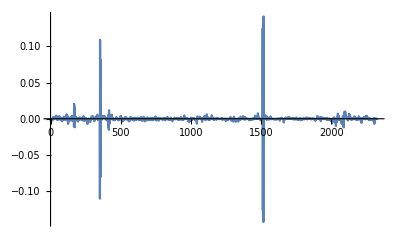

```mathematica
ListLinePlot[rsUniWeth, PlotRange->All]
```

```mathematica
(* Yea, UNI/WETH definitely not looking as extreme as ALCX/WETH ... :) *)
```

```mathematica
edistUniWeth = EstimatedDistribution[rsUniWeth, StableDistribution[1, aUW, bUW, locUW, scaleUW]]
```

StableDistribution[1,1.32783,0.0816836,-0.0000252748,0.000640944]

```mathematica
f = {1.3278285879842862,0.0816835526225623,-0.0000252748167384907,0.0006409442772706084}
```

{1.32783,0.0816836,-0.0000252748,0.000640944}

```mathematica
Export["fit.csv", f]
```

fit.csv

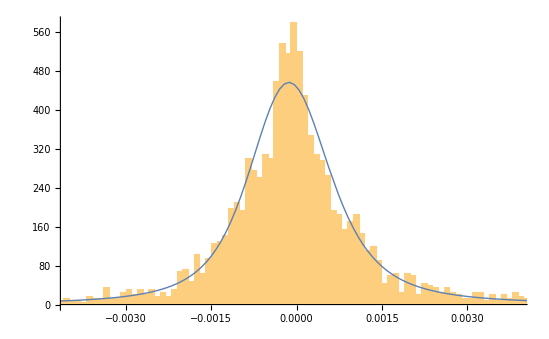

```mathematica
Show[Histogram[rsUniWeth, {0.0001}, "PDF"], Plot[PDF[edistUniWeth, x], {x, Min[rsUniWeth], Max[rsUniWeth]}, PlotRange->All, PlotStyle->Thick]]
```

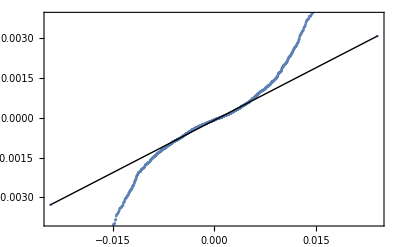

```mathematica
QuantilePlot[rsUniWeth]
```

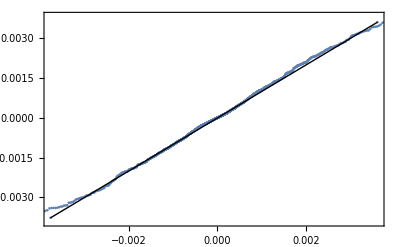

```mathematica
QuantilePlot[rsUniWeth, edistUniWeth]
```

```mathematica
(* Examine more data ... ~ 2.5 months. Don't use WETH/DAI since cron didn't start til May 19th for this pair *)
```

```mathematica
tblUniWeth90d = Import["90/data-1625069716_uni-weth-twap.csv"]
```

{{,timestamp,twap},{0,1.61878×10^9,1.4244×10^16},{1,1.61878×10^9,1.42041×10^16},{2,1.61878×10^9,1.41202×10^16},{3,1.61878×10^9,1.41232×10^16},{4,1.61885×10^9,1.11905×10^16},5940,{5946,1.62505×10^9,8.45706×10^15},{5947,1.62505×10^9,8.45105×10^15},{5948,1.62505×10^9,8.43944×10^15},{5949,1.62506×10^9,8.40945×10^15},{5950,1.62506×10^9,8.39535×10^15},{5951,1.62507×10^9,8.38014×10^15}}
 |  |  |  |

```mathematica
Length[tblUniWeth90d]
```

5952

```mathematica
FromUnixTime[tblUniWeth90d[[2]][[2]]]
```

Sun 18 Apr 2021 17:11:37GMT-4.

```mathematica
FromUnixTime[tblUniWeth90d[[Length[tblUniWeth90d]]][[2]]]
```

Wed 30 Jun 2021 11:12:11GMT-4.

```mathematica
twapsUniWeth90d = Table[tblUniWeth90d[[i]][[3]], {i, 2, Length[tblUniWeth90d]}]
```

{1.4244×10^16,1.42041×10^16,1.41202×10^16,1.41232×10^16,1.11905×10^16,1.1152×10^16,1.11664×10^16,1.11894×10^16,1.12534×10^16,1.43174×10^16,1.43461×10^16,1.43877×10^16,1.44245×10^16,1.45323×10^16,1.46054×10^16,1.46277×10^16,6.78005×10^16,1.46625×10^16,1.47173×10^16,1.47457×10^16,1.47367×10^16,1.47112×10^16,1.47093×10^16,1.46965×10^16,1.4693×10^16,1.46974×10^16,1.47074×10^16,1.46991×10^16,1.46988×10^16,1.46882×10^16,1.46469×10^16,1.45575×10^16,1.44941×10^16,1.44527×10^16,1.44296×10^16,1.44048×10^16,1.43748×10^16,1.43042×10^16,1.42377×10^16,1.41513×10^16,1.40647×10^16,1.4037×10^16,1.40033×10^16,1.3985×10^16,1.39899×10^16,1.39702×10^16,1.39903×10^16,1.4033×10^16,1.40449×10^16,1.40431×10^16,1.40417×10^16,1.40173×10^16,1.3944×10^16,1.39079×10^16,1.38472×10^16,1.38336×10^16,1.38352×10^16,1.38429×10^16,1.38433×10^16,1.38711×10^16,1.38869×10^16,1.3899×10^16,1.39186×10^16,1.3921×10^16,1.39176×10^16,1.38979×10^16,1.38774×10^16,1.3856×10^16,1.38393×10^16,1.3829×10^16,1.3808×10^16,1.37221×10^16,1.35037×10^16,1.34808×10^16,1.34925×10^16,1.34994×10^16,1.35191×10^16,1.36529×10^16,1.3682×10^16,1.37078×10^16,1.3713×10^16,1.37054×10^16,1.36837×10^16,1.36537×10^16,1.36374×10^16,1.36282×10^16,1.35991×10^16,1.3589×10^16,1.35825×10^16,1.35551×10^16,1.35337×10^16,1.35453×10^16,1.35606×10^16,1.36053×10^16,1.36494×10^16,1.36663×10^16,1.36976×10^16,1.37173×10^16,1.37111×10^16,1.37232×10^16,1.37249×10^16,1.36965×10^16,1.36601×10^16,1.36426×10^16,1.36623×10^16,1.37063×10^16,1.37625×10^16,1.38671×10^16,1.3917×10^16,1.39274×10^16,1.39312×10^16,1.39385×10^16,1.3937×10^16,1.39063×10^16,1.38837×10^16,1.38717×10^16,1.38472×10^16,1.38449×10^16,1.38347×10^16,1.38296×10^16,1.38345×10^16,1.38091×10^16,1.38004×10^16,1.37992×10^16,1.38027×10^16,1.38049×10^16,1.38449×10^16,1.39925×10^16,1.40314×10^16,1.40592×10^16,1.40792×10^16,1.40646×10^16,1.40505×10^16,1.39918×10^16,1.39149×10^16,1.38461×10^16,1.3762×10^16,1.37427×10^16,1.36956×10^16,1.36195×10^16,1.35761×10^16,1.35272×10^16,1.3509×10^16,1.35027×10^16,1.35065×10^16,1.35427×10^16,1.35926×10^16,1.36404×10^16,1.37001×10^16,1.37786×10^16,1.38932×10^16,1.4073×10^16,1.42423×10^16,1.43066×10^16,1.43399×10^16,1.44377×10^16,1.45196×10^16,1.45539×10^16,1.46053×10^16,1.4737×10^16,1.47173×10^16,1.46739×10^16,1.466×10^16,1.46774×10^16,1.46677×10^16,1.46691×10^16,1.46448×10^16,1.46154×10^16,1.45299×10^16,1.44979×10^16,1.44453×10^16,1.44064×10^16,1.44044×10^16,1.43972×10^16,1.43982×10^16,1.43944×10^16,1.43835×10^16,1.43694×10^16,1.43445×10^16,1.43263×10^16,1.43212×10^16,1.42827×10^16,1.42106×10^16,1.41886×10^16,1.41733×10^16,1.41961×10^16,1.42318×10^16,1.43313×10^16,1.44233×10^16,1.44907×10^16,1.46451×10^16,1.46994×10^16,1.47221×10^16,1.4714×10^16,1.47261×10^16,1.47393×10^16,1.48052×10^16,1.48795×10^16,1.49834×10^16,1.50446×10^16,1.50913×10^16,1.51016×10^16,1.51154×10^16,1.51545×10^16,1.51981×10^16,1.51921×10^16,1.52088×10^16,1.51617×10^16,1.507×10^16,1.49623×10^16,1.49003×10^16,1.48903×10^16,1.48698×10^16,1.48692×10^16,1.48723×10^16,1.48685×10^16,1.48635×10^16,1.48708×10^16,1.4933×10^16,1.50195×10^16,1.50942×10^16,1.51632×10^16,1.51757×10^16,1.52008×10^16,1.52135×10^16,1.52352×10^16,1.52748×10^16,1.52577×10^16,1.52058×10^16,1.51189×10^16,1.50572×10^16,1.49895×10^16,1.49228×10^16,1.49068×10^16,1.48131×10^16,1.4801×10^16,1.47933×10^16,1.47777×10^16,1.47723×10^16,1.47327×10^16,1.46801×10^16,1.45567×10^16,1.44706×10^16,1.44474×10^16,1.43825×10^16,1.43609×10^16,1.43487×10^16,1.43179×10^16,1.4305×10^16,1.4286×10^16,1.42659×10^16,1.42585×10^16,1.42228×10^16,1.42144×10^16,1.41542×10^16,1.40575×10^16,1.39924×10^16,1.39513×10^16,1.39406×10^16,1.39123×10^16,1.39041×10^16,1.39164×10^16,1.39161×10^16,1.39274×10^16,1.39542×10^16,1.39595×10^16,1.40286×10^16,1.40504×10^16,1.40556×10^16,1.40633×10^16,1.40742×10^16,1.40795×10^16,1.40795×10^16,1.41273×10^16,1.41628×10^16,1.42089×10^16,1.42533×10^16,1.42931×10^16,1.43101×10^16,1.43224×10^16,1.437×10^16,1.44052×10^16,1.44072×10^16,1.43912×10^16,1.43567×10^16,1.42971×10^16,1.42623×10^16,1.42456×10^16,1.42455×10^16,1.42573×10^16,1.42204×10^16,1.42078×10^16,1.41601×10^16,1.41336×10^16,1.41036×10^16,1.40539×10^16,1.40433×10^16,1.4041×10^16,1.40862×10^16,1.41705×10^16,1.42542×10^16,1.43073×10^16,1.43442×10^16,1.4386×10^16,1.44303×10^16,1.44369×10^16,1.44249×10^16,1.4403×10^16,1.43898×10^16,1.44036×10^16,1.44075×10^16,1.4437×10^16,1.44542×10^16,1.44466×10^16,1.44461×10^16,1.44506×10^16,1.4478×10^16,1.45394×10^16,1.4613×10^16,1.46128×10^16,1.46092×10^16,1.45577×10^16,1.45244×10^16,1.44544×10^16,1.43907×10^16,1.4363×10^16,1.43148×10^16,1.42867×10^16,1.42533×10^16,1.41895×10^16,1.41802×10^16,1.41887×10^16,1.41951×10^16,1.42173×10^16,1.42208×10^16,1.42209×10^16,1.41657×10^16,1.41317×10^16,1.40858×10^16,1.40476×10^16,1.39936×10^16,1.39299×10^16,1.39068×10^16,1.38952×10^16,1.39009×10^16,1.39101×10^16,1.3916×10^16,1.39094×10^16,1.38949×10^16,1.38598×10^16,1.37836×10^16,1.37764×10^16,1.37593×10^16,1.3759×10^16,1.37714×10^16,1.38033×10^16,1.38267×10^16,1.38458×10^16,1.38523×10^16,1.38636×10^16,1.38673×10^16,1.39035×10^16,1.39177×10^16,1.39412×10^16,1.39922×10^16,1.40212×10^16,1.398×10^16,1.39649×10^16,1.39221×10^16,1.38766×10^16,1.38544×10^16,1.38184×10^16,1.37909×10^16,1.37814×10^16,1.37912×10^16,1.3799×10^16,1.38077×10^16,1.38423×10^16,1.38676×10^16,1.38846×10^16,1.39094×10^16,1.39193×10^16,1.39304×10^16,1.39352×10^16,1.39378×10^16,1.39326×10^16,1.39256×10^16,1.39138×10^16,1.38931×10^16,1.38879×10^16,1.39108×10^16,1.39559×10^16,1.39704×10^16,1.40006×10^16,1.40176×10^16,1.40272×10^16,1.40153×10^16,1.40158×10^16,1.40186×10^16,1.40223×10^16,1.40235×10^16,1.40355×10^16,1.40463×10^16,1.40624×10^16,1.40668×10^16,1.40686×10^16,1.4059×10^16,1.40569×10^16,1.40547×10^16,1.40918×10^16,1.41025×10^16,1.41282×10^16,1.41326×10^16,1.41134×10^16,1.39936×10^16,1.39638×10^16,1.39205×10^16,1.39018×10^16,1.3859×10^16,1.38565×10^16,1.38487×10^16,1.38085×10^16,1.38037×10^16,1.38016×10^16,1.37847×10^16,1.37574×10^16,1.3741×10^16,1.37216×10^16,1.37064×10^16,1.36852×10^16,1.36869×10^16,1.3692×10^16,1.36928×10^16,1.36902×10^16,1.36826×10^16,1.36512×10^16,1.36174×10^16,1.35984×10^16,1.35974×10^16,1.35969×10^16,1.35957×10^16,1.35954×10^16,1.3607×10^16,1.36143×10^16,1.36185×10^16,1.36294×10^16,1.36429×10^16,1.36461×10^16,1.36452×10^16,1.36435×10^16,1.36479×10^16,1.36789×10^16,1.3684×10^16,1.3692×10^16,1.37253×10^16,1.37328×10^16,1.37465×10^16,1.37527×10^16,1.37546×10^16,1.37736×10^16,1.37759×10^16,1.38022×10^16,1.38294×10^16,1.38356×10^16,1.38479×10^16,1.3858×10^16,1.38642×10^16,1.38619×10^16,1.38631×10^16,1.38613×10^16,1.38637×10^16,1.38665×10^16,1.38688×10^16,1.38662×10^16,1.38408×10^16,1.38325×10^16,1.38244×10^16,1.38291×10^16,1.38736×10^16,1.39678×10^16,1.4087×10^16,1.42454×10^16,1.43564×10^16,1.44342×10^16,1.44758×10^16,1.45224×10^16,1.4509×10^16,1.44997×10^16,1.45091×10^16,1.44997×10^16,1.4509×10^16,1.45298×10^16,1.45332×10^16,1.45073×10^16,1.45184×10^16,1.45412×10^16,1.45711×10^16,1.46335×10^16,1.47338×10^16,1.47842×10^16,1.48096×10^16,1.48005×10^16,1.47802×10^16,1.47073×10^16,1.46644×10^16,1.46182×10^16,1.45558×10^16,1.45132×10^16,1.45725×10^16,1.45963×10^16,1.46307×10^16,1.46559×10^16,1.46843×10^16,1.46831×10^16,1.46697×10^16,1.46619×10^16,1.46623×10^16,1.46204×10^16,1.45925×10^16,1.45342×10^16,1.44831×10^16,1.44405×10^16,1.43935×10^16,1.44188×10^16,1.44767×10^16,1.44876×10^16,1.45003×10^16,1.45318×10^16,1.45323×10^16,1.45393×10^16,1.4531×10^16,1.45264×10^16,1.45248×10^16,1.45183×10^16,1.44951×10^16,1.44722×10^16,1.4464×10^16,1.44716×10^16,1.44877×10^16,1.45037×10^16,1.45333×10^16,1.45584×10^16,1.4598×10^16,1.46556×10^16,1.46981×10^16,1.48033×10^16,1.48334×10^16,1.48214×10^16,1.47839×10^16,1.47519×10^16,1.46919×10^16,1.46653×10^16,1.46492×10^16,1.45827×10^16,1.45573×10^16,1.45217×10^16,1.44899×10^16,1.44448×10^16,1.44315×10^16,1.44315×10^16,1.44175×10^16,1.43817×10^16,1.43751×10^16,1.43571×10^16,1.4361×10^16,1.43791×10^16,1.44169×10^16,1.449×10^16,1.45734×10^16,1.46173×10^16,1.46602×10^16,1.46594×10^16,1.46262×10^16,1.45887×10^16,1.45617×10^16,1.45475×10^16,1.45342×10^16,1.4524×10^16,1.45211×10^16,1.4518×10^16,1.4513×10^16,1.45071×10^16,1.44985×10^16,1.44833×10^16,1.45213×10^16,1.454×10^16,1.45578×10^16,1.45834×10^16,1.45966×10^16,1.45687×10^16,1.45387×10^16,1.45072×10^16,1.44175×10^16,1.43522×10^16,1.4303×10^16,1.42869×10^16,1.4286×10^16,1.42885×10^16,1.42975×10^16,1.4321×10^16,1.43335×10^16,1.43454×10^16,1.43447×10^16,1.43411×10^16,1.43346×10^16,1.43309×10^16,1.4311×10^16,1.42879×10^16,1.42637×10^16,1.42492×10^16,1.4236×10^16,1.42205×10^16,1.42211×10^16,1.42321×10^16,1.42501×10^16,1.42791×10^16,1.43297×10^16,1.43699×10^16,1.43928×10^16,1.44209×10^16,1.44362×10^16,1.44835×10^16,1.44996×10^16,1.45066×10^16,1.45161×10^16,1.45268×10^16,1.45532×10^16,1.46171×10^16,1.47025×10^16,1.48083×10^16,1.48971×10^16,1.49256×10^16,1.49835×10^16,1.50208×10^16,1.50712×10^16,1.50922×10^16,1.50989×10^16,1.51032×10^16,1.51016×10^16,1.5072×10^16,1.50402×10^16,1.50172×10^16,1.50077×10^16,1.5009×10^16,1.50158×10^16,1.503×10^16,1.50347×10^16,1.50501×10^16,1.5048×10^16,1.50434×10^16,1.50056×10^16,1.49894×10^16,1.50092×10^16,1.5104×10^16,1.51143×10^16,1.51703×10^16,1.51916×10^16,1.52113×10^16,1.52678×10^16,1.53037×10^16,1.54733×10^16,1.56226×10^16,1.57179×10^16,1.57561×10^16,1.57677×10^16,1.57702×10^16,1.57624×10^16,1.57358×10^16,1.57098×10^16,1.56785×10^16,1.56234×10^16,1.55975×10^16,1.55814×10^16,1.557×10^16,1.55846×10^16,1.56193×10^16,1.5635×10^16,1.56399×10^16,1.56392×10^16,1.5653×10^16,1.56844×10^16,1.57202×10^16,1.57381×10^16,1.57645×10^16,1.57578×10^16,1.57066×10^16,1.56357×10^16,1.55819×10^16,1.55562×10^16,1.554×10^16,1.54617×10^16,1.54387×10^16,1.54198×10^16,1.53846×10^16,1.53736×10^16,1.51719×10^16,1.51004×10^16,1.50567×10^16,1.49902×10^16,1.49453×10^16,1.49353×10^16,1.49258×10^16,1.49264×10^16,1.4923×10^16,1.49397×10^16,1.48929×10^16,1.48763×10^16,1.48577×10^16,1.48372×10^16,1.48402×10^16,1.48543×10^16,1.48667×10^16,1.48799×10^16,1.489×10^16,1.49064×10^16,1.49173×10^16,1.49359×10^16,1.49372×10^16,1.49392×10^16,1.49588×10^16,1.49641×10^16,1.49718×10^16,1.49856×10^16,1.50068×10^16,1.50125×10^16,1.50069×10^16,1.50069×10^16,1.49946×10^16,1.49574×10^16,1.49622×10^16,1.49821×10^16,1.504×10^16,1.5118×10^16,1.52474×10^16,1.53948×10^16,1.54405×10^16,1.54533×10^16,1.54593×10^16,1.54348×10^16,1.54122×10^16,1.53972×10^16,1.53796×10^16,1.5357×10^16,1.53328×10^16,1.53183×10^16,1.52626×10^16,1.52459×10^16,1.51881×10^16,1.51733×10^16,1.51551×10^16,1.51531×10^16,1.51466×10^16,1.51498×10^16,1.50823×10^16,1.50368×10^16,1.50106×10^16,1.49669×10^16,1.49431×10^16,1.49049×10^16,1.48742×10^16,1.48886×10^16,1.49106×10^16,1.49442×10^16,1.50255×10^16,1.50488×10^16,1.50753×10^16,1.51105×10^16,1.51232×10^16,1.5144×10^16,1.51375×10^16,1.51312×10^16,1.50971×10^16,1.50947×10^16,1.51031×10^16,1.5109×10^16,1.51107×10^16,1.5105×10^16,1.51109×10^16,1.51321×10^16,1.51582×10^16,1.51772×10^16,1.52788×10^16,1.52988×10^16,1.5374×10^16,1.54055×10^16,1.54326×10^16,1.55007×10^16,1.55087×10^16,1.55035×10^16,1.5495×10^16,1.55154×10^16,1.55581×10^16,1.5568×10^16,1.55608×10^16,1.55693×10^16,1.55618×10^16,1.553×10^16,1.55033×10^16,1.55353×10^16,1.55822×10^16,1.56019×10^16,1.56492×10^16,1.56551×10^16,1.56593×10^16,1.56657×10^16,1.56539×10^16,1.56066×10^16,1.55982×10^16,1.5591×10^16,1.55859×10^16,1.55756×10^16,1.55358×10^16,1.553×10^16,1.55151×10^16,1.55035×10^16,1.5487×10^16,1.54927×10^16,1.5476×10^16,1.54554×10^16,1.54365×10^16,1.54357×10^16,1.54269×10^16,1.54111×10^16,1.53976×10^16,1.53954×10^16,1.5384×10^16,1.53843×10^16,1.54061×10^16,1.54372×10^16,1.54644×10^16,1.55387×10^16,1.5598×10^16,1.57495×10^16,1.57788×10^16,1.58355×10^16,1.58536×10^16,1.58156×10^16,1.57605×10^16,1.57763×10^16,1.58035×10^16,1.58304×10^16,1.58785×10^16,1.58953×10^16,1.58887×10^16,1.5879×10^16,1.58655×10^16,1.58508×10^16,1.58102×10^16,1.5772×10^16,1.57366×10^16,1.57047×10^16,1.5694×10^16,1.56725×10^16,1.56745×10^16,1.56747×10^16,1.56854×10^16,1.56917×10^16,1.57×10^16,1.56905×10^16,1.56827×10^16,1.56482×10^16,1.56195×10^16,1.55486×10^16,1.55088×10^16,1.54917×10^16,1.54785×10^16,1.54762×10^16,1.5473×10^16,1.54727×10^16,1.54629×10^16,1.54598×10^16,1.544×10^16,1.54315×10^16,1.541×10^16,1.5397×10^16,1.53706×10^16,1.53153×10^16,1.52987×10^16,1.5288×10^16,1.52887×10^16,1.52893×10^16,1.52902×10^16,1.52804×10^16,1.52632×10^16,1.52267×10^16,1.51923×10^16,1.51387×10^16,1.51084×10^16,1.51045×10^16,1.51024×10^16,1.50874×10^16,1.50454×10^16,1.50326×10^16,1.49663×10^16,1.49524×10^16,1.49268×10^16,1.4906×10^16,1.48952×10^16,1.48648×10^16,1.48428×10^16,1.47894×10^16,1.47478×10^16,1.47386×10^16,1.47295×10^16,1.47342×10^16,1.47676×10^16,1.47805×10^16,1.47877×10^16,1.48043×10^16,1.48215×10^16,1.48285×10^16,1.48576×10^16,1.4889×10^16,1.49092×10^16,1.49809×10^16,1.4993×10^16,1.50317×10^16,1.50417×10^16,1.50384×10^16,1.50324×10^16,1.50342×10^16,1.50346×10^16,1.50327×10^16,1.50301×10^16,1.5025×10^16,1.50046×10^16,1.4991×10^16,1.4984×10^16,1.49682×10^16,1.49551×10^16,1.4911×10^16,1.48643×10^16,1.48015×10^16,1.47773×10^16,1.47747×10^16,1.47647×10^16,1.47476×10^16,1.47094×10^16,1.46969×10^16,1.46869×10^16,1.4671×10^16,1.46638×10^16,1.46494×10^16,1.46743×10^16,1.46848×10^16,1.46924×10^16,1.4691×10^16,1.46859×10^16,1.46727×10^16,1.46637×10^16,1.46592×10^16,1.46679×10^16,1.47029×10^16,1.47469×10^16,1.47677×10^16,1.4778×10^16,1.47954×10^16,1.4788×10^16,1.47664×10^16,1.47269×10^16,1.4718×10^16,1.47145×10^16,1.4721×10^16,1.47268×10^16,1.47336×10^16,1.47389×10^16,1.474×10^16,1.47436×10^16,1.47446×10^16,1.47399×10^16,1.47366×10^16,1.4724×10^16,1.46977×10^16,1.46728×10^16,1.46517×10^16,1.46383×10^16,1.4624×10^16,1.46124×10^16,1.45988×10^16,1.45888×10^16,1.45825×10^16,1.45949×10^16,1.46169×10^16,1.46718×10^16,1.46679×10^16,1.46671×10^16,1.46414×10^16,1.4616×10^16,1.4591×10^16,1.454×10^16,1.45061×10^16,1.4468×10^16,1.44042×10^16,1.44171×10^16,1.44235×10^16,1.44872×10^16,1.45261×10^16,1.45537×10^16,1.45776×10^16,1.45842×10^16,1.45922×10^16,1.4588×10^16,1.4585×10^16,1.46056×10^16,1.46106×10^16,1.46182×10^16,1.4633×10^16,1.46405×10^16,1.46362×10^16,1.46339×10^16,1.46349×10^16,1.46283×10^16,1.46216×10^16,1.46157×10^16,1.46138×10^16,1.46101×10^16,1.46061×10^16,1.46002×10^16,1.4595×10^16,1.46082×10^16,1.46088×10^16,1.46016×10^16,1.46041×10^16,1.46055×10^16,1.45956×10^16,1.45978×10^16,1.46056×10^16,1.46031×10^16,1.45988×10^16,1.45924×10^16,1.45741×10^16,1.45452×10^16,1.45213×10^16,1.44942×10^16,1.44502×10^16,1.43961×10^16,1.43962×10^16,1.43983×10^16,1.44013×10^16,1.44101×10^16,1.44237×10^16,1.44192×10^16,1.44103×10^16,1.44046×10^16,1.43942×10^16,1.43619×10^16,1.43526×10^16,1.4347×10^16,1.4333×10^16,1.43208×10^16,1.43027×10^16,1.42823×10^16,1.42612×10^16,1.42043×10^16,1.41985×10^16,1.41957×10^16,1.42072×10^16,1.42337×10^16,1.42385×10^16,1.42068×10^16,1.41913×10^16,1.41279×10^16,1.40715×10^16,1.40661×10^16,1.40469×10^16,1.4038×10^16,1.40056×10^16,1.3997×10^16,1.39924×10^16,1.39901×10^16,1.39757×10^16,1.39691×10^16,1.39682×10^16,1.39486×10^16,1.39405×10^16,1.39405×10^16,1.39412×10^16,1.39453×10^16,1.3961×10^16,1.39712×10^16,1.39718×10^16,1.3967×10^16,1.39577×10^16,1.39458×10^16,1.3943×10^16,1.39359×10^16,1.39171×10^16,1.38992×10^16,1.38768×10^16,1.38444×10^16,1.38209×10^16,1.38155×10^16,1.38053×10^16,1.38091×10^16,1.38031×10^16,1.37945×10^16,1.37856×10^16,1.37509×10^16,1.37077×10^16,1.36937×10^16,1.3689×10^16,1.36802×10^16,1.36918×10^16,1.37016×10^16,1.37026×10^16,1.36951×10^16,1.36891×10^16,1.36659×10^16,1.3658×10^16,1.36534×10^16,1.36646×10^16,1.60876×10^16,1.3671×10^16,1.36639×10^16,1.36518×10^16,1.36276×10^16,1.19101×10^16,1.35831×10^16,1.35564×10^16,1.35497×10^16,1.35488×10^16,1.35499×10^16,1.35535×10^16,1.35617×10^16,1.35708×10^16,1.35851×10^16,1.35862×10^16,1.35952×10^16,1.35975×10^16,1.35945×10^16,1.36027×10^16,1.36097×10^16,1.36123×10^16,1.36213×10^16,1.36341×10^16,1.3631×10^16,1.36296×10^16,1.36273×10^16,1.36251×10^16,1.36221×10^16,1.36204×10^16,1.36192×10^16,1.36173×10^16,1.36252×10^16,1.3654×10^16,1.36691×10^16,1.3673×10^16,1.36763×10^16,1.3677×10^16,1.36745×10^16,1.36788×10^16,1.36828×10^16,1.36949×10^16,1.36997×10^16,1.37082×10^16,1.37108×10^16,1.37127×10^16,1.37077×10^16,1.37106×10^16,1.37246×10^16,1.37336×10^16,1.3762×10^16,1.38042×10^16,1.38412×10^16,1.38937×10^16,1.39172×10^16,1.39522×10^16,1.3974×10^16,1.39713×10^16,1.39579×10^16,1.39935×10^16,1.40754×10^16,1.41652×10^16,1.43345×10^16,1.44414×10^16,1.4554×10^16,1.46003×10^16,1.459×10^16,1.45286×10^16,1.45059×10^16,1.44784×10^16,1.44386×10^16,1.44251×10^16,1.44373×10^16,1.44433×10^16,1.44551×10^16,1.44822×10^16,1.45172×10^16,1.4534×10^16,1.45213×10^16,1.45222×10^16,1.44964×10^16,1.44763×10^16,1.4471×10^16,1.44585×10^16,1.44584×10^16,1.44584×10^16,1.44564×10^16,1.44555×10^16,1.44488×10^16,1.44377×10^16,1.44428×10^16,1.44482×10^16,1.44492×10^16,1.44587×10^16,1.44696×10^16,1.44517×10^16,1.44433×10^16,1.44439×10^16,1.44354×10^16,1.44301×10^16,1.44222×10^16,1.44127×10^16,1.43742×10^16,1.43618×10^16,1.43388×10^16,1.43241×10^16,1.43295×10^16,1.43354×10^16,1.43523×10^16,1.43743×10^16,1.43933×10^16,1.44196×10^16,1.44303×10^16,1.44534×10^16,1.44152×10^16,1.44068×10^16,1.43798×10^16,1.43723×10^16,1.43741×10^16,1.43872×10^16,1.44196×10^16,1.44911×10^16,1.45279×10^16,1.45787×10^16,1.46081×10^16,1.46269×10^16,1.46109×10^16,1.46053×10^16,1.46103×10^16,1.46233×10^16,1.4634×10^16,1.46525×10^16,1.46615×10^16,1.46525×10^16,1.46298×10^16,1.46002×10^16,1.45561×10^16,1.44969×10^16,1.44729×10^16,1.44473×10^16,1.44355×10^16,1.44093×10^16,1.4385×10^16,1.43657×10^16,1.43329×10^16,1.42866×10^16,1.42559×10^16,1.42106×10^16,1.41653×10^16,1.41447×10^16,1.40723×10^16,1.40273×10^16,1.39879×10^16,1.39648×10^16,1.39437×10^16,1.39299×10^16,1.38943×10^16,1.38881×10^16,1.38825×10^16,1.38791×10^16,1.38797×10^16,1.38926×10^16,1.39008×10^16,1.38966×10^16,1.3892×10^16,1.38683×10^16,1.38459×10^16,1.382×10^16,1.38221×10^16,1.38292×10^16,1.38494×10^16,1.3847×10^16,1.38228×10^16,1.37793×10^16,1.37535×10^16,1.37309×10^16,1.37208×10^16,1.37066×10^16,1.36742×10^16,1.366×10^16,1.36267×10^16,1.36067×10^16,1.35882×10^16,1.35618×10^16,1.34674×10^16,1.34048×10^16,1.33173×10^16,1.32341×10^16,1.32032×10^16,1.31204×10^16,1.3101×10^16,1.30653×10^16,1.30241×10^16,1.29279×10^16,1.28606×10^16,1.28011×10^16,1.27813×10^16,1.27759×10^16,1.27655×10^16,1.27384×10^16,1.2721×10^16,1.26911×10^16,1.26511×10^16,1.2638×10^16,1.26288×10^16,1.26117×10^16,1.25854×10^16,1.25637×10^16,1.25168×10^16,1.24818×10^16,1.24441×10^16,1.24305×10^16,1.24021×10^16,1.2391×10^16,1.23834×10^16,1.237×10^16,1.23825×10^16,1.23731×10^16,1.23729×10^16,1.23761×10^16,1.23812×10^16,1.23714×10^16,1.23744×10^16,1.23978×10^16,1.24085×10^16,1.24257×10^16,1.24489×10^16,1.24633×10^16,1.24911×10^16,1.24996×10^16,1.25115×10^16,1.25321×10^16,1.253×10^16,1.25081×10^16,1.24939×10^16,1.24776×10^16,1.24558×10^16,1.2432×10^16,1.24221×10^16,1.24171×10^16,1.24088×10^16,1.24002×10^16,1.23892×10^16,1.23907×10^16,1.23927×10^16,1.23882×10^16,1.23833×10^16,1.2385×10^16,1.23933×10^16,1.23997×10^16,1.2417×10^16,1.24476×10^16,1.24493×10^16,1.2447×10^16,1.24447×10^16,1.24418×10^16,1.24404×10^16,1.24333×10^16,1.2413×10^16,1.23919×10^16,1.23658×10^16,1.23397×10^16,1.22946×10^16,1.2274×10^16,1.23459×10^16,1.2445×10^16,1.25171×10^16,1.26284×10^16,1.27401×10^16,1.27471×10^16,1.27096×10^16,1.26732×10^16,1.25806×10^16,1.25316×10^16,1.24679×10^16,1.23891×10^16,1.23628×10^16,1.23489×10^16,1.23605×10^16,1.24168×10^16,1.24781×10^16,1.25081×10^16,1.25218×10^16,1.25282×10^16,1.25497×10^16,1.25716×10^16,1.26014×10^16,1.26116×10^16,1.26167×10^16,1.26285×10^16,1.26377×10^16,1.26406×10^16,1.26631×10^16,1.26615×10^16,1.26667×10^16,1.2681×10^16,1.26933×10^16,1.26856×10^16,1.26906×10^16,1.26891×10^16,1.26866×10^16,1.26722×10^16,1.26753×10^16,1.27063×10^16,1.27513×10^16,1.28067×10^16,1.28551×10^16,1.29173×10^16,1.29794×10^16,1.30236×10^16,1.30616×10^16,1.31064×10^16,1.31256×10^16,1.31669×10^16,1.31942×10^16,1.32062×10^16,1.33064×10^16,1.33474×10^16,1.33912×10^16,1.34243×10^16,1.34226×10^16,1.33388×10^16,1.32123×10^16,1.30522×10^16,1.29821×10^16,1.2861×10^16,1.28182×10^16,1.28795×10^16,1.29247×10^16,1.29564×10^16,1.2987×10^16,1.29968×10^16,1.30196×10^16,1.3025×10^16,1.30276×10^16,1.30418×10^16,1.30548×10^16,1.30651×10^16,1.3076×10^16,1.30726×10^16,1.3064×10^16,1.30461×10^16,1.30356×10^16,1.30322×10^16,1.30402×10^16,1.30491×10^16,1.30664×10^16,1.30848×10^16,1.30906×10^16,1.30954×10^16,1.31095×10^16,1.31136×10^16,1.3133×10^16,1.31534×10^16,1.31685×10^16,1.31875×10^16,1.31613×10^16,1.31502×10^16,1.30809×10^16,1.30482×10^16,1.30153×10^16,1.30062×10^16,1.2984×10^16,1.29781×10^16,1.29811×10^16,1.29744×10^16,1.29812×10^16,1.30017×10^16,1.29833×10^16,1.2964×10^16,1.29548×10^16,1.29321×10^16,1.29193×10^16,1.29065×10^16,1.2885×10^16,1.28654×10^16,1.28572×10^16,1.28576×10^16,1.28801×10^16,1.29377×10^16,1.29761×10^16,1.30023×10^16,1.30124×10^16,1.30236×10^16,1.30268×10^16,1.30231×10^16,1.30191×10^16,1.3×10^16,1.29599×10^16,1.28814×10^16,1.28103×10^16,1.27494×10^16,1.2681×10^16,1.26321×10^16,1.25824×10^16,1.2562×10^16,1.25614×10^16,1.25689×10^16,1.25788×10^16,1.25917×10^16,1.26354×10^16,1.26645×10^16,1.26396×10^16,1.26262×10^16,1.25896×10^16,1.25112×10^16,1.2463×10^16,1.24347×10^16,1.24239×10^16,1.24108×10^16,1.23981×10^16,1.23916×10^16,1.23572×10^16,1.23341×10^16,1.2317×10^16,1.22879×10^16,1.22736×10^16,1.22606×10^16,1.22305×10^16,1.22056×10^16,1.21463×10^16,1.21312×10^16,1.21034×10^16,1.20545×10^16,1.2039×10^16,1.20252×10^16,1.2014×10^16,1.20077×10^16,1.20078×10^16,1.20068×10^16,1.20113×10^16,1.20162×10^16,1.20135×10^16,1.2012×10^16,1.20095×10^16,1.20043×10^16,1.1999×10^16,1.19961×10^16,1.1994×10^16,1.19927×10^16,1.1994×10^16,1.20063×10^16,1.2042×10^16,1.20588×10^16,1.20781×10^16,1.20862×10^16,1.20928×10^16,1.2094×10^16,1.21009×10^16,1.20996×10^16,1.2097×10^16,1.21007×10^16,1.21326×10^16,1.21382×10^16,1.2155×10^16,1.21693×10^16,1.21789×10^16,1.21843×10^16,1.21518×10^16,1.21384×10^16,1.21175×10^16,1.21084×10^16,1.21106×10^16,1.21124×10^16,1.21425×10^16,1.21639×10^16,1.21776×10^16,1.21759×10^16,1.21758×10^16,1.2159×10^16,1.21085×10^16,1.20843×10^16,1.20652×10^16,1.20484×10^16,1.20246×10^16,1.19902×10^16,1.19751×10^16,1.19605×10^16,1.19515×10^16,1.19467×10^16,1.19416×10^16,1.19408×10^16,1.19359×10^16,1.19295×10^16,1.19153×10^16,1.19051×10^16,1.18956×10^16,1.18807×10^16,1.18531×10^16,1.18477×10^16,1.1804×10^16,1.17518×10^16,1.17028×10^16,1.16657×10^16,1.1657×10^16,1.25328×10^16,1.16454×10^16,1.16407×10^16,1.16489×10^16,1.16516×10^16,1.07189×10^16,1.16466×10^16,1.16465×10^16,1.1642×10^16,1.16631×10^16,1.16625×10^16,1.16618×10^16,1.16602×10^16,1.16628×10^16,1.16533×10^16,1.16508×10^16,1.16531×10^16,1.16639×10^16,1.16684×10^16,1.16661×10^16,1.16594×10^16,1.16542×10^16,1.16297×10^16,1.16035×10^16,1.15893×10^16,1.15808×10^16,1.15792×10^16,1.15564×10^16,1.15294×10^16,1.15187×10^16,1.14985×10^16,1.14861×10^16,1.14592×10^16,1.14436×10^16,1.14391×10^16,1.14356×10^16,1.14391×10^16,1.14442×10^16,1.14485×10^16,1.14531×10^16,1.14466×10^16,1.14435×10^16,1.14428×10^16,1.14281×10^16,1.14178×10^16,1.13888×10^16,1.13788×10^16,1.13709×10^16,1.13757×10^16,1.13827×10^16,1.13954×10^16,1.14043×10^16,1.14298×10^16,1.14421×10^16,1.14521×10^16,1.14592×10^16,1.14663×10^16,1.14817×10^16,1.14922×10^16,1.15073×10^16,1.15308×10^16,1.15429×10^16,1.15707×10^16,1.16002×10^16,1.16247×10^16,1.16464×10^16,1.16518×10^16,1.16612×10^16,1.16709×10^16,1.16712×10^16,1.16712×10^16,1.16745×10^16,1.16757×10^16,1.16734×10^16,1.16686×10^16,1.16705×10^16,1.16681×10^16,1.16746×10^16,1.16836×10^16,1.16991×10^16,1.16995×10^16,1.1697×10^16,1.16945×10^16,1.16924×10^16,1.16882×10^16,1.16872×10^16,1.16843×10^16,1.16783×10^16,1.16796×10^16,1.16787×10^16,1.16785×10^16,1.16749×10^16,1.16748×10^16,1.16526×10^16,1.16256×10^16,1.16152×10^16,1.15983×10^16,1.15706×10^16,1.15373×10^16,1.1496×10^16,1.14717×10^16,1.14551×10^16,1.14585×10^16,1.14758×10^16,1.15035×10^16,1.15185×10^16,1.15259×10^16,1.15253×10^16,1.15238×10^16,1.15096×10^16,1.14954×10^16,1.14844×10^16,1.14607×10^16,1.14542×10^16,1.14506×10^16,1.14464×10^16,1.145×10^16,1.14536×10^16,1.1455×10^16,1.1454×10^16,1.14475×10^16,1.14339×10^16,1.14155×10^16,1.13838×10^16,1.13631×10^16,1.13523×10^16,1.13494×10^16,1.13589×10^16,1.13662×10^16,1.13647×10^16,1.13598×10^16,1.13583×10^16,1.13311×10^16,1.1325×10^16,1.1315×10^16,1.13157×10^16,1.13226×10^16,1.13309×10^16,1.13383×10^16,1.13485×10^16,1.1357×10^16,1.13621×10^16,1.13603×10^16,1.13541×10^16,1.13458×10^16,1.13395×10^16,1.13287×10^16,1.13243×10^16,1.13115×10^16,1.13025×10^16,1.12951×10^16,1.12812×10^16,1.12795×10^16,1.12331×10^16,1.12227×10^16,1.12161×10^16,1.12128×10^16,1.12108×10^16,1.12115×10^16,1.12327×10^16,1.12493×10^16,1.12528×10^16,1.12537×10^16,1.12586×10^16,1.12515×10^16,1.12524×10^16,1.12529×10^16,1.12531×10^16,1.12478×10^16,1.12388×10^16,1.12208×10^16,1.12078×10^16,1.11657×10^16,1.11173×10^16,1.10667×10^16,1.10406×10^16,1.09993×10^16,1.09812×10^16,1.09705×10^16,1.09713×10^16,1.09836×10^16,1.10081×10^16,1.10353×10^16,1.10166×10^16,1.09582×10^16,1.09077×10^16,1.08217×10^16,1.07898×10^16,1.07602×10^16,1.07246×10^16,1.0718×10^16,1.07085×10^16,1.0711×10^16,1.07083×10^16,1.07018×10^16,1.06969×10^16,1.06642×10^16,1.06371×10^16,1.06141×10^16,1.05593×10^16,1.05469×10^16,1.04905×10^16,1.04475×10^16,1.04197×10^16,1.04176×10^16,1.04195×10^16,1.04034×10^16,1.03944×10^16,1.03982×10^16,1.04016×10^16,1.04044×10^16,1.04165×10^16,1.04196×10^16,1.04185×10^16,1.04082×10^16,1.04019×10^16,1.03949×10^16,1.03895×10^16,1.03714×10^16,1.0346×10^16,1.03042×10^16,1.02769×10^16,1.02111×10^16,1.01876×10^16,1.01715×10^16,1.01525×10^16,1.01077×10^16,1.00703×10^16,1.00617×10^16,1.00553×10^16,1.00438×10^16,1.00354×10^16,1.00235×10^16,9.98962×10^15,9.98572×10^15,9.99994×10^15,1.00125×10^16,1.0042×10^16,1.00563×10^16,1.00749×10^16,1.00837×10^16,1.01278×10^16,1.01433×10^16,1.01493×10^16,1.0157×10^16,1.01607×10^16,1.01606×10^16,1.01558×10^16,1.01531×10^16,1.01471×10^16,1.01468×10^16,1.01605×10^16,1.01668×10^16,1.01729×10^16,1.01818×10^16,1.01834×10^16,1.01846×10^16,1.01863×10^16,1.01886×10^16,1.01876×10^16,1.01877×10^16,1.01876×10^16,1.01854×10^16,1.01836×10^16,1.01828×10^16,1.0178×10^16,1.01671×10^16,1.01325×10^16,1.01003×10^16,1.00749×10^16,1.00482×10^16,1.00427×10^16,1.00336×10^16,1.00372×10^16,1.00428×10^16,1.0042×10^16,1.00414×10^16,1.00408×10^16,1.00385×10^16,1.00379×10^16,1.00358×10^16,1.00329×10^16,1.00321×10^16,1.00308×10^16,1.00346×10^16,1.00364×10^16,1.00388×10^16,1.00453×10^16,1.00454×10^16,1.00422×10^16,1.00403×10^16,1.00547×10^16,1.00685×10^16,1.00718×10^16,1.008×10^16,1.00956×10^16,1.0099×10^16,1.01043×10^16,1.01208×10^16,1.01673×10^16,1.01799×10^16,1.01858×10^16,1.0193×10^16,1.0197×10^16,1.01867×10^16,1.01817×10^16,1.01619×10^16,1.01366×10^16,1.0128×10^16,1.01129×10^16,1.01094×10^16,1.00979×10^16,1.00748×10^16,1.00661×10^16,1.00215×10^16,1.00026×10^16,9.989×10^15,9.95086×10^15,9.93537×10^15,9.92173×10^15,9.914×10^15,9.90945×10^15,9.90189×10^15,9.8758×10^15,9.8294×10^15,9.81345×10^15,9.78522×10^15,9.78064×10^15,9.77131×10^15,9.74342×10^15,9.74479×10^15,9.75637×10^15,9.76249×10^15,9.76731×10^15,9.7762×10^15,9.76169×10^15,9.74117×10^15,9.67016×10^15,9.56944×10^15,9.55707×10^15,9.53777×10^15,9.5322×10^15,9.51717×10^15,9.51778×10^15,9.51435×10^15,9.51533×10^15,9.48035×10^15,9.4598×10^15,9.4277×10^15,9.37746×10^15,9.33872×10^15,9.30375×10^15,9.28297×10^15,9.25225×10^15,9.20421×10^15,9.16056×10^15,9.15182×10^15,9.21265×10^15,9.2582×10^15,9.26549×10^15,9.27794×10^15,9.27763×10^15,9.27452×10^15,9.25833×10^15,9.24783×10^15,9.22947×10^15,9.21686×10^15,9.20355×10^15,9.20575×10^15,9.20784×10^15,9.20929×10^15,9.21486×10^15,9.22169×10^15,9.22778×10^15,9.23172×10^15,9.24941×10^15,9.26864×10^15,9.29715×10^15,9.31397×10^15,9.33815×10^15,9.35322×10^15,9.34955×10^15,9.34647×10^15,9.34433×10^15,9.34251×10^15,9.34689×10^15,9.36431×10^15,9.37188×10^15,9.38365×10^15,9.34541×10^15,9.33384×10^15,9.32037×10^15,9.31467×10^15,9.31284×10^15,9.31662×10^15,9.32313×10^15,9.33211×10^15,9.33694×10^15,9.34362×10^15,9.36388×10^15,9.37009×10^15,9.37782×10^15,9.3637×10^15,9.35715×10^15,9.34365×10^15,9.29344×10^15,9.27053×10^15,9.25267×10^15,9.26989×10^15,9.2763×10^15,9.29341×10^15,9.29856×10^15,9.31211×10^15,9.31528×10^15,9.31632×10^15,9.30416×10^15,9.29754×10^15,9.28726×10^15,9.26118×10^15,9.2531×10^15,9.25129×10^15,9.25099×10^15,9.2498×10^15,9.26341×10^15,9.25447×10^15,9.24931×10^15,9.24521×10^15,9.24225×10^15,9.21057×10^15,9.21285×10^15,9.22013×10^15,9.21246×10^15,9.20303×10^15,9.21128×10^15,9.21306×10^15,9.22275×10^15,9.23745×10^15,9.25573×10^15,9.28982×10^15,9.29257×10^15,9.3271×10^15,9.361×10^15,9.37682×10^15,9.37286×10^15,9.35911×10^15,9.34119×10^15,9.34421×10^15,9.38197×10^15,9.43733×10^15,9.50504×10^15,9.60535×10^15,9.61072×10^15,9.58157×10^15,9.54975×10^15,9.53768×10^15,9.52848×10^15,9.54621×10^15,9.59037×10^15,9.68532×10^15,9.78648×10^15,9.96428×10^15,1.00493×10^16,1.00337×10^16,1.00329×10^16,1.00054×10^16,9.99717×10^15,9.98485×10^15,9.91713×10^15,9.90288×10^15,9.87086×10^15,9.84306×10^15,9.82123×10^15,9.79522×10^15,9.82317×10^15,9.8333×10^15,9.84568×10^15,9.86214×10^15,9.87251×10^15,9.85659×10^15,9.86386×10^15,9.86217×10^15,9.85391×10^15,9.85295×10^15,9.8599×10^15,9.85515×10^15,9.87974×10^15,9.90877×10^15,9.9432×10^15,9.97194×10^15,1.00037×10^16,1.00248×10^16,1.00163×10^16,1.00085×10^16,1.00011×10^16,1.0006×10^16,1.00119×10^16,1.00143×10^16,1.00112×10^16,1.0015×10^16,1.00017×10^16,1.00046×10^16,1.00155×10^16,1.0016×10^16,9.99712×10^15,9.9871×10^15,9.95538×10^15,9.93023×10^15,9.89525×10^15,9.81018×10^15,9.77243×10^15,9.71125×10^15,9.67633×10^15,9.65536×10^15,9.64835×10^15,9.64085×10^15,9.65416×10^15,9.67097×10^15,9.67849×10^15,9.68697×10^15,9.6888×10^15,9.67948×10^15,9.6963×10^15,9.7082×10^15,9.7175×10^15,9.73155×10^15,9.76743×10^15,9.82603×10^15,9.85707×10^15,9.90855×10^15,9.91938×10^15,9.93156×10^15,9.95748×10^15,9.96295×10^15,9.96169×10^15,9.96311×10^15,9.97083×10^15,9.96341×10^15,9.94554×10^15,9.93073×10^15,9.9233×10^15,9.93397×10^15,9.9467×10^15,1.0008×10^16,1.00797×10^16,1.0208×10^16,1.02763×10^16,1.02816×10^16,1.02877×10^16,1.02765×10^16,1.02558×10^16,1.02185×10^16,1.01569×10^16,1.01115×10^16,1.00425×10^16,1.00119×10^16,9.9981×10^15,9.96903×10^15,9.94983×10^15,9.92169×10^15,9.90469×10^15,9.89287×10^15,9.87981×10^15,9.87416×10^15,9.9042×10^15,9.91924×10^15,9.93994×10^15,9.94419×10^15,9.94751×10^15,9.93997×10^15,9.93695×10^15,9.92096×10^15,9.923×10^15,9.92122×10^15,9.92252×10^15,9.9355×10^15,9.95144×10^15,9.95098×10^15,9.96754×10^15,9.98088×10^15,9.98324×10^15,9.98331×10^15,9.98681×10^15,9.9937×10^15,9.97299×10^15,9.95708×10^15,9.94913×10^15,9.93223×10^15,9.9312×10^15,9.92049×10^15,9.92668×10^15,9.93485×10^15,9.94143×10^15,9.94216×10^15,9.97996×10^15,1.00043×10^16,1.00126×10^16,1.0009×10^16,1.00031×10^16,1.00012×10^16,9.99619×10^15,9.99456×10^15,9.98735×10^15,9.98467×10^15,9.97522×10^15,9.96725×10^15,9.97032×10^15,9.97717×10^15,9.99252×10^15,9.989×10^15,9.99116×10^15,9.98632×10^15,9.98554×10^15,9.98026×10^15,9.97087×10^15,9.9578×10^15,9.93399×10^15,9.92427×10^15,9.90306×10^15,9.88383×10^15,9.87619×10^15,9.86546×10^15,9.85032×10^15,9.8323×10^15,9.79322×10^15,9.77651×10^15,9.74969×10^15,9.73455×10^15,9.73661×10^15,9.74684×10^15,9.75579×10^15,9.77048×10^15,9.8131×10^15,9.82722×10^15,9.82773×10^15,9.82242×10^15,9.81648×10^15,9.80973×10^15,9.79919×10^15,9.79832×10^15,9.79618×10^15,9.79177×10^15,9.79134×10^15,9.79123×10^15,9.79214×10^15,9.79223×10^15,9.79922×10^15,9.80755×10^15,9.81969×10^15,9.83598×10^15,9.85265×10^15,9.87357×10^15,9.89902×10^15,9.92148×10^15,9.93175×10^15,9.95341×10^15,9.97716×10^15,1.00456×10^16,1.00987×10^16,1.01781×10^16,1.01976×10^16,1.02325×10^16,1.02812×10^16,1.0299×10^16,1.0358×10^16,1.03666×10^16,1.03486×10^16,1.03243×10^16,1.032×10^16,1.0307×10^16,1.02995×10^16,1.02783×10^16,1.02347×10^16,1.02186×10^16,1.01712×10^16,1.01465×10^16,1.01322×10^16,1.01234×10^16,1.01177×10^16,1.01177×10^16,1.01173×10^16,1.01151×10^16,1.01137×10^16,1.0111×10^16,1.01025×10^16,1.01018×10^16,1.00936×10^16,1.00867×10^16,1.00757×10^16,1.00546×10^16,1.00491×10^16,1.00206×10^16,1.00155×10^16,1.00058×10^16,9.99204×10^15,9.98889×10^15,9.9856×10^15,9.98169×10^15,9.9825×10^15,9.98654×10^15,1.00015×10^16,1.00105×10^16,1.00247×10^16,1.0059×10^16,1.00977×10^16,1.01141×10^16,1.01048×10^16,1.01005×10^16,1.00965×10^16,1.00896×10^16,1.00864×10^16,1.00806×10^16,1.00684×10^16,1.00504×10^16,1.00419×10^16,1.00342×10^16,1.00309×10^16,1.00245×10^16,1.00098×10^16,9.9985×10^15,9.99524×10^15,9.96885×10^15,9.97337×10^15,9.99389×10^15,1.00012×10^16,1.00013×10^16,1.00151×10^16,1.0015×10^16,9.99958×10^15,9.99841×10^15,9.99692×10^15,9.9755×10^15,9.95736×10^15,9.95194×10^15,9.93681×10^15,9.93624×10^15,9.9352×10^15,9.93689×10^15,9.93855×10^15,9.94698×10^15,9.95488×10^15,9.96355×10^15,9.97478×10^15,9.97762×10^15,9.97087×10^15,9.96437×10^15,9.95677×10^15,9.95628×10^15,9.95774×10^15,9.96368×10^15,9.96127×10^15,9.95875×10^15,9.95772×10^15,9.96722×10^15,9.99083×10^15,1.0019×10^16,1.0052×10^16,1.01058×10^16,1.01387×10^16,1.01549×10^16,1.01709×10^16,1.01969×10^16,1.02031×10^16,1.02068×10^16,1.02223×10^16,1.02264×10^16,1.0221×10^16,1.02143×10^16,1.02162×10^16,1.02081×10^16,1.01962×10^16,1.02008×10^16,1.02054×10^16,1.01994×10^16,1.02046×10^16,1.02166×10^16,1.02263×10^16,1.02355×10^16,1.02432×10^16,1.02549×10^16,1.0242×10^16,1.02211×10^16,1.02082×10^16,1.02006×10^16,1.019×10^16,1.01714×10^16,1.0174×10^16,1.01826×10^16,1.02013×10^16,1.02127×10^16,1.02405×10^16,1.02459×10^16,1.02501×10^16,1.02466×10^16,1.02346×10^16,1.02105×10^16,1.0219×10^16,1.0221×10^16,1.0229×10^16,1.02561×10^16,1.02454×10^16,1.02496×10^16,1.02655×10^16,1.02833×10^16,1.02962×10^16,1.03119×10^16,1.03186×10^16,1.0319×10^16,1.03152×10^16,1.03003×10^16,1.02962×10^16,1.02591×10^16,1.02429×10^16,1.02337×10^16,1.02194×10^16,1.02241×10^16,1.0227×10^16,1.02279×10^16,1.02289×10^16,1.02228×10^16,1.02109×10^16,1.0212×10^16,1.07671×10^16,1.02198×10^16,1.0226×10^16,1.0229×10^16,1.02335×10^16,9.43657×10^15,1.02267×10^16,1.02186×10^16,1.02042×10^16,1.02005×10^16,1.01984×10^16,1.01987×10^16,1.01985×10^16,1.01916×10^16,1.01795×10^16,1.0166×10^16,1.01529×10^16,1.0144×10^16,1.0144×10^16,1.01486×10^16,1.0152×10^16,1.01577×10^16,1.01551×10^16,1.01485×10^16,1.01202×10^16,1.00936×10^16,1.00824×10^16,1.00764×10^16,1.00656×10^16,1.00611×10^16,1.00462×10^16,1.00384×10^16,1.00214×10^16,1.00092×10^16,1.00094×10^16,1.00178×10^16,1.00222×10^16,1.00375×10^16,1.00526×10^16,1.00636×10^16,1.00812×10^16,1.00915×10^16,1.00979×10^16,1.01005×10^16,1.01056×10^16,1.0108×10^16,1.01203×10^16,1.01288×10^16,1.01362×10^16,1.01523×10^16,1.01597×10^16,1.01669×10^16,1.0172×10^16,1.01719×10^16,1.0163×10^16,1.01562×10^16,1.01566×10^16,1.01754×10^16,1.01756×10^16,1.01852×10^16,1.01706×10^16,1.01654×10^16,1.01296×10^16,1.01258×10^16,1.01225×10^16,1.01089×10^16,1.01226×10^16,1.01333×10^16,1.01407×10^16,1.01423×10^16,1.0133×10^16,1.01277×10^16,1.01332×10^16,1.01513×10^16,1.0169×10^16,1.0193×10^16,1.01998×10^16,1.02014×10^16,1.01973×10^16,1.01829×10^16,1.01692×10^16,1.0158×10^16,1.01557×10^16,1.01536×10^16,1.01615×10^16,1.01732×10^16,1.01876×10^16,1.01949×10^16,1.02019×10^16,1.0206×10^16,1.02065×10^16,1.0206×10^16,1.0201×10^16,1.01836×10^16,1.01686×10^16,1.01577×10^16,1.01606×10^16,1.01603×10^16,1.01651×10^16,1.0174×10^16,1.01852×10^16,1.0198×10^16,1.02289×10^16,1.0252×10^16,1.02729×10^16,1.02712×10^16,1.02692×10^16,1.02666×10^16,1.02618×10^16,1.02703×10^16,1.02762×10^16,1.02798×10^16,1.02875×10^16,1.02984×10^16,1.02852×10^16,1.02831×10^16,1.02802×10^16,1.02814×10^16,1.02829×10^16,1.02807×10^16,1.02776×10^16,1.02719×10^16,1.02511×10^16,1.02345×10^16,1.02329×10^16,1.02394×10^16,1.02507×10^16,1.02521×10^16,1.0261×10^16,1.02686×10^16,1.0274×10^16,1.0274×10^16,1.02996×10^16,1.03158×10^16,1.03372×10^16,1.03576×10^16,1.03535×10^16,1.03496×10^16,1.03403×10^16,1.03321×10^16,1.03313×10^16,1.03299×10^16,1.03305×10^16,1.03165×10^16,1.02957×10^16,1.0286×10^16,1.02586×10^16,1.02506×10^16,1.02509×10^16,1.02792×10^16,1.0301×10^16,1.03484×10^16,1.0362×10^16,1.03684×10^16,1.0372×10^16,1.03758×10^16,1.03738×10^16,1.03729×10^16,1.03696×10^16,1.03651×10^16,1.03562×10^16,1.03588×10^16,1.03564×10^16,1.03592×10^16,1.03628×10^16,1.03628×10^16,1.03469×10^16,1.03341×10^16,1.03179×10^16,1.03103×10^16,1.03035×10^16,1.02735×10^16,1.02698×10^16,1.02809×10^16,1.02969×10^16,1.029×10^16,1.02995×10^16,1.0312×10^16,1.0307×10^16,1.02789×10^16,1.02516×10^16,1.02446×10^16,1.02338×10^16,1.02233×10^16,1.02336×10^16,1.0241×10^16,1.02436×10^16,1.0251×10^16,1.02481×10^16,1.02471×10^16,1.02468×10^16,1.02462×10^16,1.02375×10^16,1.02402×10^16,1.02412×10^16,1.02428×10^16,1.0245×10^16,1.02695×10^16,1.02716×10^16,1.02441×10^16,1.01959×10^16,1.01491×10^16,1.01022×10^16,1.00053×10^16,9.99621×10^15,9.99827×10^15,9.98996×10^15,9.94124×10^15,9.82752×10^15,9.74172×10^15,9.64066×10^15,9.61361×10^15,9.57941×10^15,9.54085×10^15,9.52089×10^15,9.52393×10^15,9.52784×10^15,9.55049×10^15,9.58143×10^15,9.61753×10^15,9.64198×10^15,9.62795×10^15,9.56211×10^15,9.51558×10^15,9.50177×10^15,9.48064×10^15,9.47065×10^15,9.46201×10^15,9.48254×10^15,9.50299×10^15,9.54349×10^15,9.57369×10^15,9.62983×10^15,9.69022×10^15,9.69708×10^15,9.71714×10^15,9.73131×10^15,9.7507×10^15,9.76694×10^15,9.77493×10^15,9.79449×10^15,9.813×10^15,9.82455×10^15,9.84092×10^15,9.84722×10^15,9.85041×10^15,9.83411×10^15,9.81226×10^15,9.79408×10^15,9.76248×10^15,9.70064×10^15,9.68925×10^15,9.68186×10^15,9.67377×10^15,9.65388×10^15,9.63198×10^15,9.60074×10^15,9.58159×10^15,9.56443×10^15,9.51258×10^15,9.4801×10^15,9.49568×10^15,9.50277×10^15,9.50594×10^15,9.54554×10^15,9.55711×10^15,9.57137×10^15,9.58109×10^15,9.59337×10^15,9.5977×10^15,9.609×10^15,9.61423×10^15,9.62062×10^15,9.61753×10^15,9.61113×10^15,9.59289×10^15,9.59085×10^15,9.59004×10^15,9.59197×10^15,9.59591×10^15,9.63221×10^15,9.64779×10^15,9.65232×10^15,9.66631×10^15,9.67585×10^15,9.66941×10^15,9.66745×10^15,9.6594×10^15,9.66843×10^15,9.66968×10^15,9.67603×10^15,9.69431×10^15,9.70796×10^15,9.72721×10^15,9.73359×10^15,9.7308×10^15,9.69545×10^15,9.6835×10^15,9.6724×10^15,9.65584×10^15,9.65567×10^15,9.66268×10^15,9.65289×10^15,9.63121×10^15,9.61219×10^15,9.56568×10^15,9.562×10^15,9.55569×10^15,9.55181×10^15,9.54082×10^15,9.52548×10^15,9.52043×10^15,9.5104×10^15,9.50163×10^15,9.46479×10^15,9.4644×10^15,9.45922×10^15,9.4469×10^15,9.44567×10^15,9.46441×10^15,9.46637×10^15,9.45946×10^15,9.46519×10^15,9.46171×10^15,9.464×10^15,9.46196×10^15,9.46732×10^15,9.45207×10^15,9.44883×10^15,9.44556×10^15,9.43656×10^15,9.42413×10^15,9.41993×10^15,9.41065×10^15,9.39995×10^15,9.39647×10^15,9.39357×10^15,9.39011×10^15,9.39944×10^15,9.4068×10^15,1.25553×10^16,9.40969×10^15,9.42691×10^15,9.43796×10^15,9.4644×10^15,6.95814×10^15,9.51697×10^15,9.54258×10^15,9.52649×10^15,9.51339×10^15,9.48817×10^15,9.47512×10^15,9.47233×10^15,9.48841×10^15,9.49669×10^15,9.50837×10^15,9.52369×10^15,9.52407×10^15,9.51611×10^15,9.51668×10^15,9.5256×10^15,9.53435×10^15,9.53736×10^15,9.54155×10^15,9.54184×10^15,9.52142×10^15,9.50758×10^15,9.49233×10^15,9.49386×10^15,9.49288×10^15,9.49716×10^15,9.50177×10^15,9.51162×10^15,9.51878×10^15,9.52937×10^15,9.55225×10^15,9.55432×10^15,9.55464×10^15,9.55709×10^15,9.55374×10^15,9.54693×10^15,9.54645×10^15,9.54189×10^15,9.53688×10^15,9.53226×10^15,9.52963×10^15,9.52273×10^15,9.51215×10^15,9.50878×10^15,9.51316×10^15,9.51481×10^15,9.518×10^15,9.52641×10^15,9.52019×10^15,9.48548×10^15,9.4339×10^15,9.39625×10^15,9.26842×10^15,9.2018×10^15,9.14426×10^15,9.12352×10^15,9.09105×10^15,9.05597×10^15,9.03365×10^15,9.00993×10^15,8.95673×10^15,8.95745×10^15,8.97886×10^15,8.99104×10^15,8.99637×10^15,8.99829×10^15,9.00261×10^15,9.01859×10^15,9.03408×10^15,9.03149×10^15,9.02942×10^15,9.01569×10^15,8.9959×10^15,8.97435×10^15,8.93585×10^15,8.94×10^15,8.93108×10^15,8.9318×10^15,8.93583×10^15,8.95241×10^15,8.9493×10^15,8.95451×10^15,8.97114×10^15,8.97735×10^15,9.00053×10^15,9.01059×10^15,9.01561×10^15,9.00558×10^15,9.00619×10^15,9.00595×10^15,8.99238×10^15,9.00049×10^15,9.00877×10^15,9.00526×10^15,9.00358×10^15,9.00226×10^15,8.97661×10^15,8.97056×10^15,8.97406×10^15,8.97082×10^15,8.97587×10^15,8.99595×10^15,9.0051×10^15,9.00608×10^15,9.00298×10^15,8.99563×10^15,8.9847×10^15,8.94791×10^15,8.89641×10^15,8.87085×10^15,8.84368×10^15,8.84702×10^15,8.84711×10^15,8.83793×10^15,8.78412×10^15,8.75237×10^15,8.69775×10^15,8.67979×10^15,8.67778×10^15,8.71182×10^15,8.74131×10^15,8.78907×10^15,8.81342×10^15,8.8139×10^15,8.81552×10^15,8.81612×10^15,8.81743×10^15,8.81087×10^15,8.81043×10^15,8.80641×10^15,8.80523×10^15,8.78748×10^15,8.77753×10^15,8.77544×10^15,8.77914×10^15,8.79043×10^15,8.80075×10^15,8.81934×10^15,8.82253×10^15,8.82465×10^15,8.81551×10^15,8.81977×10^15,8.82284×10^15,8.83373×10^15,8.82822×10^15,8.82986×10^15,8.82247×10^15,8.81998×10^15,8.83322×10^15,8.84423×10^15,8.85415×10^15,8.87669×10^15,8.88291×10^15,8.89063×10^15,8.88716×10^15,8.88691×10^15,8.87584×10^15,8.87338×10^15,8.87508×10^15,8.88152×10^15,8.88015×10^15,8.88241×10^15,8.87939×10^15,8.89226×10^15,8.89513×10^15,8.90082×10^15,8.89247×10^15,8.89637×10^15,8.89407×10^15,8.89561×10^15,8.89685×10^15,8.90685×10^15,8.89415×10^15,8.89032×10^15,8.89122×10^15,8.89155×10^15,8.89446×10^15,8.91012×10^15,8.90861×10^15,8.90496×10^15,8.90429×10^15,8.8997×10^15,8.89809×10^15,8.8994×10^15,8.9003×10^15,8.89054×10^15,8.89055×10^15,8.88921×10^15,8.88843×10^15,8.89251×10^15,8.89904×10^15,8.89029×10^15,8.88963×10^15,8.87905×10^15,8.86966×10^15,8.89097×10^15,8.9038×10^15,8.90336×10^15,8.91674×10^15,8.91687×10^15,8.91097×10^15,8.90912×10^15,8.912×10^15,8.90056×10^15,8.89876×10^15,8.8897×10^15,8.89134×10^15,8.89049×10^15,8.89839×10^15,8.90903×10^15,8.92203×10^15,8.93303×10^15,8.937×10^15,8.94069×10^15,8.941×10^15,8.94227×10^15,8.94477×10^15,8.94748×10^15,8.94594×10^15,8.92507×10^15,8.91017×10^15,8.90011×10^15,8.87555×10^15,8.86626×10^15,8.84584×10^15,8.81299×10^15,8.7917×10^15,8.76209×10^15,8.71841×10^15,8.70576×10^15,8.67069×10^15,8.64089×10^15,8.56608×10^15,8.48966×10^15,8.44827×10^15,8.38365×10^15,8.36346×10^15,8.34139×10^15,8.3513×10^15,8.35198×10^15,8.35427×10^15,8.35189×10^15,8.33608×10^15,8.31644×10^15,8.30099×10^15,8.25669×10^15,8.17023×10^15,8.08628×10^15,7.98351×10^15,7.88036×10^15,7.8003×10^15,7.77419×10^15,7.76162×10^15,7.76373×10^15,7.79183×10^15,7.82011×10^15,7.81928×10^15,7.80418×10^15,7.78562×10^15,7.76473×10^15,7.71757×10^15,7.64606×10^15,7.62599×10^15,7.63484×10^15,7.69374×10^15,7.75664×10^15,7.82911×10^15,7.90359×10^15,7.92658×10^15,7.93033×10^15,7.92898×10^15,7.93055×10^15,7.91689×10^15,7.89579×10^15,7.8807×10^15,7.85781×10^15,7.83174×10^15,7.80507×10^15,7.7947×10^15,7.7914×10^15,7.79164×10^15,7.80202×10^15,7.8155×10^15,7.84193×10^15,7.86715×10^15,7.87416×10^15,7.88575×10^15,7.90042×10^15,7.92531×10^15,7.9611×10^15,7.97466×10^15,7.99948×10^15,8.03529×10^15,8.04733×10^15,8.03862×10^15,8.0287×10^15,8.02669×10^15,8.01374×10^15,8.00122×10^15,8.00045×10^15,8.01859×10^15,8.02694×10^15,8.02464×10^15,8.01994×10^15,8.0144×10^15,8.00296×10^15,7.98459×10^15,7.98651×10^15,8.0026×10^15,8.02236×10^15,8.03995×10^15,8.07032×10^15,8.09221×10^15,8.1029×10^15,8.12286×10^15,8.12579×10^15,8.12874×10^15,8.12425×10^15,8.12291×10^15,8.12067×10^15,8.13141×10^15,8.13903×10^15,8.16275×10^15,8.17954×10^15,8.19817×10^15,8.21386×10^15,8.21451×10^15,8.21745×10^15,8.22255×10^15,8.21956×10^15,8.22728×10^15,8.24961×10^15,8.25583×10^15,8.27521×10^15,8.30302×10^15,8.31829×10^15,8.3486×10^15,8.36991×10^15,8.39291×10^15,8.42376×10^15,8.43443×10^15,8.43942×10^15,8.4327×10^15,8.43192×10^15,8.44138×10^15,8.43981×10^15,8.43861×10^15,8.43977×10^15,8.43866×10^15,8.42107×10^15,8.44803×10^15,8.46514×10^15,8.4912×10^15,8.52667×10^15,8.54634×10^15,8.61102×10^15,8.63757×10^15,8.66298×10^15,8.67672×10^15,8.69582×10^15,8.71654×10^15,8.70763×10^15,8.69901×10^15,8.69492×10^15,8.67937×10^15,8.67053×10^15,8.6784×10^15,8.68334×10^15,8.68514×10^15,8.69128×10^15,8.71538×10^15,8.74909×10^15,8.81024×10^15,8.85672×10^15,8.90383×10^15,8.92637×10^15,8.96602×10^15,8.96647×10^15,8.98927×10^15,9.03339×10^15,9.07702×10^15,9.16182×10^15,9.22178×10^15,9.29057×10^15,9.31187×10^15,9.31222×10^15,9.33211×10^15,9.3403×10^15,1.11783×10^16,9.34249×10^15,9.35048×10^15,9.32979×10^15,9.32011×10^15,7.989×10^15,9.31919×10^15,9.33021×10^15,9.35743×10^15,9.37506×10^15,9.38576×10^15,9.38029×10^15,9.38358×10^15,9.35902×10^15,9.33616×10^15,9.3208×10^15,9.31146×10^15,9.31366×10^15,9.31615×10^15,9.32664×10^15,9.34642×10^15,9.3644×10^15,9.37245×10^15,9.4083×10^15,9.44123×10^15,9.50931×10^15,9.54368×10^15,9.60206×10^15,9.62118×10^15,9.60747×10^15,9.55509×10^15,9.52718×10^15,9.49361×10^15,9.4672×10^15,9.46445×10^15,9.46247×10^15,9.45211×10^15,9.43139×10^15,9.40741×10^15,9.36293×10^15,9.34817×10^15,9.33937×10^15,9.32311×10^15,9.32038×10^15,9.33175×10^15,9.33085×10^15,9.33674×10^15,9.37117×10^15,9.38362×10^15,9.37129×10^15,9.3762×10^15,9.40468×10^15,9.42594×10^15,9.44338×10^15,9.49172×10^15,9.52102×10^15,9.55794×10^15,9.55506×10^15,9.54522×10^15,9.51883×10^15,9.50366×10^15,9.47685×10^15,9.44535×10^15,9.4145×10^15,9.38193×10^15,9.35465×10^15,9.34503×10^15,9.31643×10^15,9.26234×10^15,9.23993×10^15,9.20353×10^15,9.15623×10^15,9.13377×10^15,9.1457×10^15,9.13831×10^15,9.13818×10^15,9.14489×10^15,9.14144×10^15,9.11929×10^15,9.10049×10^15,9.09453×10^15,9.09344×10^15,9.09381×10^15,9.09061×10^15,9.09843×10^15,9.11217×10^15,9.11859×10^15,9.12935×10^15,9.1724×10^15,9.19999×10^15,9.22355×10^15,9.27039×10^15,9.2764×10^15,9.27705×10^15,9.28129×10^15,9.31612×10^15,9.33339×10^15,9.36348×10^15,9.36901×10^15,9.37504×10^15,9.39856×10^15,9.39961×10^15,9.40609×10^15,9.42683×10^15,9.42751×10^15,9.38984×10^15,9.38316×10^15,9.38239×10^15,9.37696×10^15,9.37144×10^15,9.37123×10^15,9.37627×10^15,9.36881×10^15,9.3705×10^15,9.38913×10^15,9.39698×10^15,9.39548×10^15,9.40086×10^15,9.39494×10^15,9.38013×10^15,9.35932×10^15,9.34468×10^15,9.31588×10^15,9.30857×10^15,9.3175×10^15,9.31969×10^15,9.33437×10^15,9.36919×10^15,9.39767×10^15,9.40861×10^15,9.41625×10^15,9.4248×10^15,9.44081×10^15,9.44651×10^15,9.45744×10^15,9.46892×10^15,9.48107×10^15,9.49363×10^15,9.49984×10^15,9.49819×10^15,9.49359×10^15,9.48616×10^15,9.47482×10^15,9.48114×10^15,9.48504×10^15,9.48539×10^15,9.48679×10^15,9.49626×10^15,9.50708×10^15,9.52551×10^15,9.53972×10^15,9.55408×10^15,9.55813×10^15,9.56929×10^15,9.57987×10^15,9.55463×10^15,9.54177×10^15,9.52033×10^15,9.48282×10^15,9.46423×10^15,9.45626×10^15,9.4587×10^15,9.46766×10^15,9.47576×10^15,9.48253×10^15,9.48772×10^15,9.49552×10^15,9.50929×10^15,9.53042×10^15,9.51648×10^15,9.50055×10^15,9.47575×10^15,9.43698×10^15,9.42572×10^15,9.41532×10^15,9.42977×10^15,9.42691×10^15,9.4427×10^15,9.44667×10^15,9.45603×10^15,9.4559×10^15,9.49312×10^15,9.48875×10^15,9.49764×10^15,9.5288×10^15,9.53401×10^15,9.54522×10^15,9.55068×10^15,9.54754×10^15,9.53612×10^15,9.5368×10^15,9.53614×10^15,9.52848×10^15,9.52772×10^15,9.52335×10^15,9.50468×10^15,9.49907×10^15,9.50185×10^15,9.52372×10^15,9.56256×10^15,9.63439×10^15,9.74822×10^15,9.84341×10^15,9.939×10^15,1.00194×10^16,1.00679×10^16,1.01086×10^16,1.01238×10^16,1.01419×10^16,1.01453×10^16,1.01259×10^16,1.01055×10^16,1.01007×10^16,1.00728×10^16,1.00671×10^16,1.00592×10^16,1.00392×10^16,1.00078×10^16,9.9933×10^15,9.99008×10^15,9.98171×10^15,9.96979×10^15,9.97023×10^15,9.95762×10^15,9.94493×10^15,9.93627×10^15,9.9233×10^15,9.92102×10^15,9.91161×10^15,9.91024×10^15,9.91762×10^15,9.94087×10^15,9.95482×10^15,9.9791×10^15,9.99584×10^15,1.00154×10^16,1.00343×10^16,1.00512×10^16,1.0072×10^16,1.00763×10^16,1.00755×10^16,1.00733×10^16,1.00751×10^16,1.00778×10^16,1.00874×10^16,1.00979×10^16,1.01099×10^16,1.01203×10^16,1.01438×10^16,1.01756×10^16,1.02191×10^16,1.02613×10^16,1.02839×10^16,1.03232×10^16,1.0341×10^16,1.03499×10^16,1.03509×10^16,1.03489×10^16,1.03328×10^16,1.03241×10^16,1.03251×10^16,1.03204×10^16,1.03085×10^16,1.02995×10^16,1.02972×10^16,1.02871×10^16,1.02856×10^16,1.02903×10^16,1.02943×10^16,1.02993×10^16,1.03189×10^16,1.03547×10^16,1.03636×10^16,1.03786×10^16,1.03933×10^16,1.04138×10^16,1.04354×10^16,1.04479×10^16,1.04773×10^16,1.04989×10^16,1.04978×10^16,1.04858×10^16,1.04781×10^16,1.0459×10^16,1.04418×10^16,1.04447×10^16,1.04533×10^16,1.04612×10^16,1.04725×10^16,1.04689×10^16,1.04676×10^16,1.04596×10^16,1.04446×10^16,1.04093×10^16,1.03827×10^16,1.03646×10^16,1.03545×10^16,1.03459×10^16,1.03374×10^16,1.03318×10^16,1.03124×10^16,1.03088×10^16,1.0313×10^16,1.03272×10^16,1.03446×10^16,1.03742×10^16,1.0385×10^16,1.03959×10^16,1.03988×10^16,1.03876×10^16,1.03787×10^16,1.03703×10^16,1.03712×10^16,1.03692×10^16,1.0374×10^16,1.03955×10^16,1.04133×10^16,1.0409×10^16,1.04055×10^16,1.039×10^16,1.03804×10^16,1.03786×10^16,1.03867×10^16,1.04066×10^16,1.04422×10^16,1.04623×10^16,1.0526×10^16,1.05542×10^16,1.05946×10^16,1.06452×10^16,1.0663×10^16,1.06977×10^16,1.07025×10^16,1.06907×10^16,1.06544×10^16,1.06203×10^16,1.05455×10^16,1.04964×10^16,1.04763×10^16,1.04626×10^16,1.0454×10^16,1.04437×10^16,1.04297×10^16,1.04147×10^16,1.03799×10^16,1.0355×10^16,1.03372×10^16,1.0333×10^16,1.03348×10^16,1.03426×10^16,1.03562×10^16,1.03766×10^16,1.03891×10^16,1.03966×10^16,1.04073×10^16,1.04154×10^16,1.04174×10^16,1.04167×10^16,1.04072×10^16,1.03797×10^16,1.03586×10^16,1.03403×10^16,1.03788×10^16,1.03896×10^16,1.0425×10^16,1.04351×10^16,1.04382×10^16,1.04338×10^16,1.04284×10^16,1.04194×10^16,1.04042×10^16,1.03916×10^16,1.03616×10^16,1.03506×10^16,1.0355×10^16,1.03559×10^16,1.0397×10^16,1.04527×10^16,1.03401×10^16,1.05552×10^16,1.0582×10^16,1.06399×10^16,1.06697×10^16,1.08388×10^16,1.07131×10^16,1.0723×10^16,1.07375×10^16,1.07419×10^16,1.07532×10^16,1.07818×10^16,1.08111×10^16,1.08398×10^16,1.08411×10^16,1.08563×10^16,1.08642×10^16,1.08679×10^16,1.08594×10^16,1.08559×10^16,1.08358×10^16,1.08101×10^16,1.08053×10^16,1.08015×10^16,1.08069×10^16,1.0809×10^16,1.08144×10^16,1.0798×10^16,1.07878×10^16,1.07462×10^16,1.07166×10^16,1.07005×10^16,1.06964×10^16,1.06939×10^16,1.06947×10^16,1.07007×10^16,1.06944×10^16,1.06831×10^16,1.06799×10^16,1.06752×10^16,1.06711×10^16,1.06794×10^16,1.06901×10^16,1.07112×10^16,1.07259×10^16,1.07371×10^16,1.07399×10^16,1.07388×10^16,1.07359×10^16,1.0728×10^16,1.0718×10^16,1.0701×10^16,1.06938×10^16,1.06934×10^16,1.06957×10^16,1.06927×10^16,1.0689×10^16,1.06815×10^16,1.06832×10^16,1.06835×10^16,1.0682×10^16,1.06754×10^16,1.06501×10^16,1.06358×10^16,1.06299×10^16,1.06391×10^16,1.06594×10^16,1.06908×10^16,1.07303×10^16,1.07445×10^16,1.07453×10^16,1.07383×10^16,1.07136×10^16,1.07013×10^16,1.06942×10^16,1.06857×10^16,1.0653×10^16,1.06341×10^16,1.06194×10^16,1.06072×10^16,1.0595×10^16,1.05963×10^16,1.05957×10^16,1.05887×10^16,1.05904×10^16,1.06012×10^16,1.05994×10^16,1.05985×10^16,1.06063×10^16,1.05922×10^16,1.05771×10^16,1.05482×10^16,1.05384×10^16,1.05071×10^16,1.04587×10^16,1.04006×10^16,1.03292×10^16,1.02916×10^16,1.02239×10^16,1.01795×10^16,1.01592×10^16,1.01529×10^16,1.01424×10^16,1.01071×10^16,1.01052×10^16,1.01035×10^16,1.01079×10^16,1.00869×10^16,1.00766×10^16,1.00686×10^16,1.00466×10^16,1.00295×10^16,1.00163×10^16,9.9986×10^15,9.97978×10^15,9.95792×10^15,9.91415×10^15,9.90958×10^15,9.9074×10^15,9.9078×10^15,9.90334×10^15,9.89406×10^15,9.89614×10^15,9.89464×10^15,9.90024×10^15,9.91026×10^15,9.94063×10^15,9.95062×10^15,9.96089×10^15,9.97326×10^15,9.98683×10^15,9.98894×10^15,9.99567×10^15,1.00326×10^16,1.00419×10^16,1.00514×10^16,1.00607×10^16,1.00693×10^16,1.00766×10^16,1.00853×10^16,1.00996×10^16,1.01057×10^16,1.00976×10^16,1.00746×10^16,1.00427×10^16,1.00108×10^16,9.98001×10^15,9.97206×10^15,9.9632×10^15,9.96505×10^15,9.9752×10^15,9.98603×10^15,9.99502×10^15,1.00129×10^16,1.00424×10^16,1.00696×10^16,1.00795×10^16,1.008×10^16,1.00831×10^16,1.00911×10^16,1.01023×10^16,1.0127×10^16,1.01502×10^16,1.01729×10^16,1.0197×10^16,1.02222×10^16,1.02788×10^16,1.0337×10^16,1.03592×10^16,1.0358×10^16,1.03428×10^16,1.03405×10^16,1.03376×10^16,1.03271×10^16,1.03249×10^16,1.03324×10^16,1.03244×10^16,1.03103×10^16,1.03028×10^16,1.03025×10^16,1.03071×10^16,1.0314×10^16,1.03293×10^16,1.03324×10^16,1.03564×10^16,9.27572×10^15,1.03432×10^16,1.03361×10^16,1.03567×10^16,1.03563×10^16,1.12319×10^16,1.03661×10^16,1.03643×10^16,1.03545×10^16,1.03512×10^16,1.03359×10^16,1.03186×10^16,1.03134×10^16,1.03067×10^16,1.03092×10^16,1.03285×10^16,1.03707×10^16,1.03826×10^16,1.03933×10^16,1.04065×10^16,1.04184×10^16,1.04514×10^16,1.04686×10^16,1.04816×10^16,1.04945×10^16,1.05043×10^16,1.05212×10^16,1.05501×10^16,1.05767×10^16,1.06047×10^16,1.06205×10^16,1.06524×10^16,1.06776×10^16,1.0715×10^16,1.07388×10^16,1.07605×10^16,1.07792×10^16,1.07821×10^16,1.07856×10^16,1.07913×10^16,1.08101×10^16,1.08218×10^16,1.08196×10^16,1.08206×10^16,1.08142×10^16,1.0795×10^16,1.07774×10^16,1.07734×10^16,1.07685×10^16,1.07696×10^16,1.07659×10^16,1.0763×10^16,1.076×10^16,1.07613×10^16,1.07354×10^16,1.07204×10^16,1.0692×10^16,1.0656×10^16,1.06051×10^16,1.06589×10^16,1.05292×10^16,1.04865×10^16,1.04577×10^16,1.04223×10^16,1.02639×10^16,1.03849×10^16,1.03845×10^16,1.03894×10^16,1.03868×10^16,1.03761×10^16,1.03097×10^16,1.03036×10^16,1.03097×10^16,1.03075×10^16,1.03033×10^16,1.03524×10^16,1.03526×10^16,1.03509×10^16,1.03611×10^16,1.03617×10^16,1.03871×10^16,1.0388×10^16,1.03901×10^16,1.0392×10^16,1.03933×10^16,1.04538×10^16,1.04471×10^16,1.04386×10^16,1.04419×10^16,1.04502×10^16,1.04477×10^16,1.04532×10^16,1.04624×10^16,1.0457×10^16,1.04481×10^16,1.04522×10^16,1.0456×10^16,1.04512×10^16,1.04435×10^16,1.04204×10^16,1.04054×10^16,1.03931×10^16,1.03758×10^16,1.03645×10^16,1.03636×10^16,1.03495×10^16,1.03416×10^16,1.03312×10^16,1.03257×10^16,1.03198×10^16,1.03109×10^16,1.03035×10^16,1.03029×10^16,1.03119×10^16,1.03224×10^16,1.0337×10^16,1.03579×10^16,1.03732×10^16,1.03881×10^16,1.04037×10^16,1.041×10^16,1.04198×10^16,1.04354×10^16,1.04384×10^16,1.04461×10^16,1.04491×10^16,1.04518×10^16,1.04546×10^16,1.0456×10^16,1.04561×10^16,1.04536×10^16,1.04372×10^16,1.04286×10^16,1.04054×10^16,1.03985×10^16,1.03969×10^16,1.03941×10^16,1.03839×10^16,1.03764×10^16,1.03736×10^16,1.03581×10^16,1.03443×10^16,1.03309×10^16,1.03191×10^16,1.03203×10^16,1.03243×10^16,1.03371×10^16,1.03767×10^16,1.0389×10^16,1.04051×10^16,1.04169×10^16,1.0451×10^16,1.04556×10^16,1.04644×10^16,1.04777×10^16,1.04754×10^16,1.04645×10^16,1.04554×10^16,1.04493×10^16,1.04509×10^16,1.04498×10^16,1.04344×10^16,1.04328×10^16,1.04236×10^16,1.03889×10^16,1.03689×10^16,1.03569×10^16,1.03386×10^16,1.03282×10^16,1.03081×10^16,1.02963×10^16,1.02921×10^16,1.02938×10^16,1.02907×10^16,1.02938×10^16,1.02991×10^16,1.03044×10^16,1.03107×10^16,1.0331×10^16,1.03443×10^16,1.0348×10^16,1.03621×10^16,1.03629×10^16,1.03595×10^16,1.03611×10^16,1.03616×10^16,1.03846×10^16,1.03904×10^16,1.03948×10^16,1.03984×10^16,1.03873×10^16,1.03789×10^16,1.03699×10^16,1.03687×10^16,1.03677×10^16,1.03664×10^16,1.03652×10^16,1.03654×10^16,1.03645×10^16,1.03559×10^16,1.03518×10^16,1.03295×10^16,1.03233×10^16,1.03185×10^16,1.03204×10^16,1.03108×10^16,1.03079×10^16,1.0299×10^16,1.02792×10^16,1.02586×10^16,1.02216×10^16,1.02035×10^16,1.01933×10^16,1.01805×10^16,1.01793×10^16,1.01764×10^16,1.01844×10^16,1.0191×10^16,1.02156×10^16,1.02285×10^16,1.0239×10^16,1.02534×10^16,1.02568×10^16,1.02508×10^16,1.02486×10^16,1.02418×10^16,1.02343×10^16,1.02343×10^16,1.02366×10^16,1.02393×10^16,1.02511×10^16,1.02635×10^16,1.02649×10^16,1.02664×10^16,1.02661×10^16,1.02578×10^16,1.0246×10^16,1.02444×10^16,1.02378×10^16,1.02258×10^16,1.02128×10^16,1.02006×10^16,1.01747×10^16,1.01634×10^16,1.01588×10^16,1.01718×10^16,1.01807×10^16,1.0192×10^16,1.01976×10^16,1.02×10^16,1.02141×10^16,1.02153×10^16,1.02089×10^16,1.02036×10^16,1.01967×10^16,1.01845×10^16,1.01746×10^16,1.01629×10^16,1.01629×10^16,1.01518×10^16,1.01473×10^16,1.0135×10^16,1.01286×10^16,1.01205×10^16,1.01187×10^16,1.01147×10^16,1.01201×10^16,1.01347×10^16,1.01383×10^16,1.014×10^16,1.01452×10^16,1.01499×10^16,1.01488×10^16,1.01562×10^16,1.01581×10^16,1.01634×10^16,1.01597×10^16,1.01569×10^16,1.01392×10^16,1.01242×10^16,1.0113×10^16,1.01×10^16,1.0111×10^16,1.01145×10^16,1.01138×10^16,1.01116×10^16,1.01086×10^16,1.00971×10^16,1.01022×10^16,1.01144×10^16,1.01316×10^16,1.01385×10^16,1.01313×10^16,1.01359×10^16,1.01371×10^16,1.01354×10^16,1.01448×10^16,1.01659×10^16,1.0157×10^16,1.01455×10^16,1.0138×10^16,1.01083×10^16,1.00973×10^16,1.00864×10^16,1.00727×10^16,1.00692×10^16,1.0058×10^16,1.00408×10^16,1.00321×10^16,1.00331×10^16,1.00342×10^16,1.00515×10^16,1.00778×10^16,1.00804×10^16,1.00928×10^16,1.00939×10^16,1.00906×10^16,1.00876×10^16,1.00863×10^16,1.00503×10^16,1.00373×10^16,1.00321×10^16,1.00271×10^16,1.00224×10^16,1.00235×10^16,1.00284×10^16,1.00319×10^16,1.00331×10^16,1.00357×10^16,1.00285×10^16,1.00094×10^16,9.99433×10^15,9.98227×10^15,9.9728×10^15,9.96418×10^15,9.94256×10^15,9.95434×10^15,9.96902×10^15,9.9791×10^15,9.99438×10^15,9.98884×10^15,9.982×10^15,9.97086×10^15,9.95526×10^15,9.94937×10^15,9.95601×10^15,9.9591×10^15,9.95464×10^15,9.94775×10^15,9.93679×10^15,9.9163×10^15,9.90624×10^15,9.89896×10^15,9.89075×10^15,9.88664×10^15,9.88296×10^15,9.86653×10^15,9.86681×10^15,9.86048×10^15,9.85721×10^15,9.85768×10^15,9.8694×10^15,9.87508×10^15,9.88682×10^15,9.88745×10^15,9.89557×10^15,9.89955×10^15,9.90251×10^15,9.90949×10^15,9.91453×10^15,9.90646×10^15,9.89361×10^15,9.88485×10^15,9.86476×10^15,9.84741×10^15,9.86033×10^15,9.86375×10^15,9.86691×10^15,9.86561×10^15,9.85804×10^15,9.84128×10^15,9.84211×10^15,9.84522×10^15,9.84863×10^15,9.84567×10^15,9.84572×10^15,9.84117×10^15,9.83074×10^15,9.82881×10^15,9.83481×10^15,9.84441×10^15,9.85397×10^15,9.85841×10^15,9.85828×10^15,9.8618×10^15,9.86747×10^15,9.89991×10^15,9.91347×10^15,9.92241×10^15,9.9164×10^15,9.91029×10^15,9.88718×10^15,9.87468×10^15,9.86925×10^15,9.86372×10^15,9.85481×10^15,9.84876×10^15,9.85292×10^15,9.85507×10^15,9.85751×10^15,9.86139×10^15,9.86116×10^15,9.84336×10^15,9.8437×10^15,9.84469×10^15,9.84832×10^15,9.84758×10^15,9.85004×10^15,9.82487×10^15,9.81427×10^15,9.80491×10^15,9.79739×10^15,9.8014×10^15,9.81399×10^15,9.81713×10^15,9.82384×10^15,9.82857×10^15,9.8334×10^15,9.83106×10^15,9.82887×10^15,9.82773×10^15,9.82274×10^15,9.81887×10^15,9.81868×10^15,9.81842×10^15,9.81844×10^15,9.81917×10^15,9.81907×10^15,9.81872×10^15,9.81421×10^15,9.81517×10^15,9.81619×10^15,9.81248×10^15,9.8068×10^15,9.80344×10^15,9.79695×10^15,9.78304×10^15,9.77846×10^15,9.77834×10^15,9.77607×10^15,9.77384×10^15,9.77569×10^15,9.78286×10^15,9.79108×10^15,9.80207×10^15,9.80274×10^15,9.81069×10^15,9.8128×10^15,9.80786×10^15,9.7922×10^15,9.77812×10^15,9.76965×10^15,9.75851×10^15,9.75495×10^15,9.75011×10^15,9.73953×10^15,9.71935×10^15,9.70099×10^15,9.69804×10^15,9.69435×10^15,9.69582×10^15,9.70259×10^15,9.71368×10^15,9.71876×10^15,9.72847×10^15,9.73709×10^15,9.7546×10^15,9.76963×10^15,9.77635×10^15,9.78142×10^15,9.79031×10^15,9.80354×10^15,9.82344×10^15,9.84043×10^15,9.8394×10^15,9.83841×10^15,9.83009×10^15,9.82004×10^15,9.80759×10^15,9.79943×10^15,9.78521×10^15,9.76989×10^15,9.76876×10^15,9.76698×10^15,9.76575×10^15,9.76594×10^15,9.76481×10^15,9.75503×10^15,9.74985×10^15,9.74197×10^15,9.73757×10^15,9.73034×10^15,9.72349×10^15,9.71841×10^15,9.71848×10^15,9.73235×10^15,9.74199×10^15,9.7524×10^15,9.75531×10^15,9.74227×10^15,9.73055×10^15,9.72353×10^15,9.71185×10^15,9.70911×10^15,9.69772×10^15,9.68955×10^15,9.66469×10^15,9.63085×10^15,9.61126×10^15,9.59549×10^15,9.58338×10^15,9.57478×10^15,9.56147×10^15,9.54724×10^15,9.53428×10^15,9.52851×10^15,9.52577×10^15,9.5228×10^15,9.52357×10^15,9.52646×10^15,9.52886×10^15,9.53481×10^15,9.54809×10^15,9.55012×10^15,9.55885×10^15,9.56406×10^15,9.56339×10^15,9.56108×10^15,9.55646×10^15,9.54898×10^15,9.5491×10^15,9.55401×10^15,9.55471×10^15,9.55702×10^15,9.56233×10^15,9.5615×10^15,9.55986×10^15,9.55858×10^15,9.55822×10^15,9.55222×10^15,9.55035×10^15,9.54718×10^15,9.54543×10^15,9.55236×10^15,9.55765×10^15,9.57054×10^15,9.58185×10^15,9.58028×10^15,9.56755×10^15,9.56379×10^15,9.55623×10^15,9.54634×10^15,9.54298×10^15,9.53422×10^15,9.53063×10^15,9.52507×10^15,9.51972×10^15,9.51276×10^15,9.50869×10^15,9.49991×10^15,9.49907×10^15,9.49412×10^15,9.4918×10^15,9.49011×10^15,9.50104×10^15,9.51432×10^15,9.53642×10^15,9.54423×10^15,9.55244×10^15,9.54397×10^15,9.53592×10^15,9.53154×10^15,9.5242×10^15,9.52048×10^15,9.51825×10^15,9.51662×10^15,9.51728×10^15,9.51367×10^15,9.50752×10^15,9.50327×10^15,9.4915×10^15,9.48675×10^15,9.47576×10^15,9.46552×10^15,9.46303×10^15,9.44654×10^15,9.44318×10^15,9.45274×10^15,9.47696×10^15,9.48229×10^15,9.51677×10^15,9.56033×10^15,9.58594×10^15,9.60053×10^15,9.60624×10^15,9.62024×10^15,9.62833×10^15,9.6305×10^15,9.63108×10^15,9.63225×10^15,9.63665×10^15,9.64056×10^15,9.64192×10^15,9.64745×10^15,9.64817×10^15,9.64456×10^15,9.64156×10^15,9.6399×10^15,9.63929×10^15,9.63906×10^15,9.64061×10^15,9.64757×10^15,9.6594×10^15,9.66593×10^15,9.66891×10^15,9.66928×10^15,9.67075×10^15,9.66278×10^15,9.65003×10^15,9.61828×10^15,9.60642×10^15,9.59209×10^15,9.57803×10^15,9.57243×10^15,9.54462×10^15,9.49919×10^15,9.47563×10^15,9.44997×10^15,9.44383×10^15,9.41723×10^15,9.41022×10^15,9.38365×10^15,9.37146×10^15,9.36312×10^15,9.34689×10^15,9.3345×10^15,9.32371×10^15,9.33535×10^15,9.34913×10^15,9.34781×10^15,9.35802×10^15,9.3401×10^15,9.32571×10^15,9.31273×10^15,9.30973×10^15,9.31026×10^15,9.30705×10^15,9.3026×10^15,9.29147×10^15,9.29733×10^15,9.29739×10^15,9.29863×10^15,9.30341×10^15,9.30949×10^15,9.30997×10^15,9.3159×10^15,9.31585×10^15,9.31265×10^15,9.31304×10^15,9.31619×10^15,9.31899×10^15,9.32505×10^15,9.33073×10^15,9.32817×10^15,9.32545×10^15,9.31707×10^15,9.30981×10^15,9.30185×10^15,9.30021×10^15,9.29403×10^15,9.28928×10^15,9.28229×10^15,9.26461×10^15,9.25504×10^15,9.24335×10^15,9.24129×10^15,9.24116×10^15,9.2335×10^15,9.22615×10^15,9.19572×10^15,9.15912×10^15,9.097×10^15,9.07823×10^15,9.08571×10^15,9.09227×10^15,9.10349×10^15,9.133×10^15,9.14034×10^15,9.14584×10^15,9.15127×10^15,9.15043×10^15,9.15251×10^15,9.16357×10^15,9.17534×10^15,9.18697×10^15,9.19743×10^15,9.2074×10^15,9.21704×10^15,9.23099×10^15,9.25679×10^15,9.28074×10^15,9.28804×10^15,9.29266×10^15,9.30206×10^15,9.31946×10^15,9.33041×10^15,9.33901×10^15,9.33623×10^15,9.33627×10^15,9.33412×10^15,9.33198×10^15,9.32776×10^15,9.33038×10^15,9.32923×10^15,9.32707×10^15,9.3175×10^15,9.31027×10^15,9.29215×10^15,9.2539×10^15,9.22683×10^15,9.21123×10^15,9.21029×10^15,9.2201×10^15,9.23071×10^15,9.24195×10^15,9.24602×10^15,9.2509×10^15,9.24806×10^15,9.25006×10^15,9.26563×10^15,9.27238×10^15,9.28134×10^15,9.29126×10^15,9.30229×10^15,9.33171×10^15,9.34138×10^15,9.36258×10^15,9.39159×10^15,9.40431×10^15,9.39977×10^15,9.39469×10^15,9.37626×10^15,9.35899×10^15,9.35169×10^15,9.34874×10^15,9.34592×10^15,9.34472×10^15,9.35609×10^15,9.38201×10^15,9.40093×10^15,9.41645×10^15,9.43093×10^15,9.48861×10^15,9.48482×10^15,9.47546×10^15,9.47355×10^15,9.47211×10^15,9.47629×10^15,9.48142×10^15,9.48646×10^15,9.4915×10^15,9.50759×10^15,9.50614×10^15,9.50484×10^15,9.5081×10^15,9.51996×10^15,9.50586×10^15,9.50354×10^15,9.50095×10^15,9.49875×10^15,9.49316×10^15,9.4882×10^15,9.47961×10^15,9.46285×10^15,9.45683×10^15,9.45256×10^15,9.45058×10^15,9.44783×10^15,9.44932×10^15,9.44905×10^15,9.44728×10^15,9.44771×10^15,9.45469×10^15,9.45947×10^15,9.46957×10^15,9.48002×10^15,9.51256×10^15,9.55899×10^15,9.59917×10^15,9.61317×10^15,9.61735×10^15,9.62192×10^15,9.62164×10^15,9.62147×10^15,9.62202×10^15,9.62351×10^15,9.63855×10^15,9.64757×10^15,9.64913×10^15,9.64407×10^15,9.63824×10^15,9.62684×10^15,9.6165×10^15,9.60739×10^15,9.58952×10^15,9.58906×10^15,9.58195×10^15,9.57688×10^15,9.57263×10^15,9.57404×10^15,9.57441×10^15,9.57414×10^15,9.5714×10^15,9.56461×10^15,9.56116×10^15,9.5623×10^15,9.56306×10^15,9.56638×10^15,9.57173×10^15,9.57633×10^15,9.57292×10^15,9.56627×10^15,9.56026×10^15,9.54914×10^15,9.55357×10^15,9.55222×10^15,9.55644×10^15,9.5598×10^15,9.57258×10^15,9.57362×10^15,9.57534×10^15,9.57987×10^15,9.57956×10^15,9.57718×10^15,9.5768×10^15,9.5756×10^15,9.57434×10^15,9.57339×10^15,9.57262×10^15,9.57148×10^15,9.57018×10^15,9.56936×10^15,9.56797×10^15,9.56713×10^15,9.56405×10^15,9.56176×10^15,9.55669×10^15,9.55234×10^15,9.55073×10^15,9.54776×10^15,9.54734×10^15,9.54694×10^15,9.54682×10^15,9.5464×10^15,9.54635×10^15,9.54959×10^15,9.55036×10^15,9.55064×10^15,9.55087×10^15,9.55444×10^15,9.55241×10^15,9.55486×10^15,9.55986×10^15,9.5454×10^15,9.53613×10^15,9.53313×10^15,9.52375×10^15,9.52156×10^15,9.52184×10^15,9.52381×10^15,9.52443×10^15,9.52525×10^15,9.52631×10^15,9.52624×10^15,9.526×10^15,9.52575×10^15,9.52555×10^15,9.52422×10^15,9.52059×10^15,9.5121×10^15,9.50353×10^15,9.49515×10^15,9.49208×10^15,9.49166×10^15,9.49547×10^15,9.49639×10^15,9.48513×10^15,9.46314×10^15,9.4319×10^15,9.4128×10^15,9.41004×10^15,9.40422×10^15,9.40128×10^15,9.39309×10^15,9.3916×10^15,9.38927×10^15,9.38949×10^15,9.38991×10^15,9.39034×10^15,9.38743×10^15,9.37167×10^15,9.36874×10^15,9.35755×10^15,9.34323×10^15,9.33004×10^15,9.31735×10^15,9.31389×10^15,9.31338×10^15,9.31262×10^15,9.31164×10^15,9.30809×10^15,9.3067×10^15,9.30556×10^15,9.30573×10^15,9.30529×10^15,9.30299×10^15,9.30068×10^15,9.29826×10^15,9.29735×10^15,9.3013×10^15,9.32331×10^15,9.33273×10^15,9.34868×10^15,9.35401×10^15,9.34292×10^15,9.33486×10^15,9.3233×10^15,9.31112×10^15,9.28493×10^15,9.28408×10^15,9.28407×10^15,9.28176×10^15,9.27021×10^15,9.266×10^15,9.26369×10^15,9.26122×10^15,9.26173×10^15,9.26021×10^15,9.25066×10^15,9.24295×10^15,9.20764×10^15,9.20588×10^15,9.20573×10^15,9.20883×10^15,9.21748×10^15,9.23036×10^15,9.25644×10^15,9.2759×10^15,9.28672×10^15,9.29172×10^15,9.28864×10^15,9.27421×10^15,9.265×10^15,9.2492×10^15,9.24215×10^15,9.23283×10^15,9.22109×10^15,9.18238×10^15,9.16667×10^15,9.14891×10^15,9.13782×10^15,9.12947×10^15,9.11373×10^15,9.10975×10^15,9.09639×10^15,9.08403×10^15,9.06562×10^15,9.05708×10^15,9.04753×10^15,9.03795×10^15,9.02984×10^15,9.01868×10^15,9.00838×10^15,8.98561×10^15,8.96104×10^15,8.93493×10^15,8.89945×10^15,8.90018×10^15,8.90584×10^15,8.91259×10^15,8.92101×10^15,8.92122×10^15,8.91928×10^15,8.915×10^15,8.9129×10^15,8.90803×10^15,8.9075×10^15,8.89384×10^15,8.89032×10^15,8.8813×10^15,8.87675×10^15,8.87782×10^15,8.90323×10^15,8.90823×10^15,8.91721×10^15,8.92053×10^15,8.9211×10^15,8.9149×10^15,8.91528×10^15,8.91284×10^15,8.92044×10^15,8.91823×10^15,8.91528×10^15,8.91269×10^15,8.91492×10^15,8.91307×10^15,8.91241×10^15,8.91392×10^15,8.91561×10^15,8.91715×10^15,8.93012×10^15,8.96305×10^15,8.97177×10^15,8.97735×10^15,8.98431×10^15,8.99137×10^15,9.00225×10^15,9.00118×10^15,8.9993×10^15,8.99762×10^15,8.98735×10^15,8.98442×10^15,8.98683×10^15,8.98887×10^15,8.98894×10^15,9.01128×10^15,9.01309×10^15,9.00515×10^15,9.00838×10^15,9.00622×10^15,9.00222×10^15,9.00488×10^15,9.00894×10^15,9.00683×10^15,9.00709×10^15,9.00469×10^15,9.00148×10^15,9.00133×10^15,9.00043×10^15,8.9994×10^15,8.99591×10^15,8.99509×10^15,8.99295×10^15,8.99179×10^15,8.99205×10^15,8.99217×10^15,8.99205×10^15,8.99192×10^15,8.99168×10^15,8.98758×10^15,8.98524×10^15,8.97481×10^15,8.96562×10^15,8.96101×10^15,8.94826×10^15,8.94082×10^15,8.92271×10^15,8.92272×10^15,8.92244×10^15,8.91958×10^15,8.9173×10^15,8.90815×10^15,8.90041×10^15,8.89744×10^15,8.88363×10^15,8.88017×10^15,8.87564×10^15,8.87666×10^15,8.87608×10^15,8.87304×10^15,8.8668×10^15,8.86429×10^15,8.85963×10^15,8.85116×10^15,8.84572×10^15,8.83777×10^15,8.83079×10^15,8.82848×10^15,8.8256×10^15,8.82647×10^15,8.82827×10^15,8.83232×10^15,8.82965×10^15,8.82695×10^15,8.82144×10^15,8.8169×10^15,8.81139×10^15,8.80843×10^15,8.80852×10^15,8.80862×10^15,8.80856×10^15,8.80756×10^15,8.80827×10^15,8.82294×10^15,8.82926×10^15,8.84415×10^15,8.88164×10^15,8.91339×10^15,8.94117×10^15,8.94987×10^15,8.9704×10^15,8.98095×10^15,8.9874×10^15,8.99651×10^15,9.00128×10^15,9.01142×10^15,9.02026×10^15,9.02213×10^15,9.03149×10^15,9.0369×10^15,9.04108×10^15,9.0467×10^15,9.05461×10^15,9.0729×10^15,9.10766×10^15,9.1233×10^15,9.19203×10^15,9.21301×10^15,9.25094×10^15,9.25134×10^15,9.25233×10^15,9.25647×10^15,9.25849×10^15,9.26607×10^15,9.27188×10^15,9.27414×10^15,9.26977×10^15,9.26609×10^15,9.25955×10^15,9.25818×10^15,9.25602×10^15,9.25996×10^15,9.25273×10^15,9.24664×10^15,9.24164×10^15,9.23092×10^15,9.21782×10^15,9.20052×10^15,9.19179×10^15,9.18889×10^15,9.18823×10^15,9.18498×10^15,9.18976×10^15,9.19162×10^15,9.19474×10^15,9.20199×10^15,9.206×10^15,9.21157×10^15,9.21994×10^15,9.21485×10^15,1.04388×10^16,9.20047×10^15,9.19303×10^15,9.19025×10^15,9.18673×10^15,7.96762×10^15,9.17613×10^15,9.16721×10^15,9.16322×10^15,9.16279×10^15,9.15931×10^15,9.15683×10^15,9.1611×10^15,9.16156×10^15,9.16262×10^15,9.16567×10^15,9.16676×10^15,9.16793×10^15,9.17207×10^15,9.21761×10^15,9.25546×10^15,9.26819×10^15,9.26938×10^15,9.27943×10^15,9.27538×10^15,9.27175×10^15,9.27484×10^15,9.28177×10^15,9.2697×10^15,9.26184×10^15,9.25869×10^15,9.25217×10^15,9.2552×10^15,9.28037×10^15,9.29957×10^15,9.31223×10^15,9.31483×10^15,9.31896×10^15,9.31347×10^15,9.31283×10^15,9.31205×10^15,9.30789×10^15,9.30227×10^15,9.29881×10^15,9.2889×10^15,9.28261×10^15,9.28268×10^15,9.28277×10^15,9.28284×10^15,9.28326×10^15,9.2835×10^15,9.27704×10^15,9.27516×10^15,9.28477×10^15,9.28645×10^15,9.2937×10^15,9.32256×10^15,9.33082×10^15,9.34625×10^15,9.34943×10^15,9.35034×10^15,9.34589×10^15,9.34384×10^15,9.34364×10^15,9.34354×10^15,9.34089×10^15,9.33553×10^15,9.33342×10^15,9.33149×10^15,9.32955×10^15,9.33078×10^15,9.33133×10^15,9.33082×10^15,9.33072×10^15,9.33036×10^15,9.32491×10^15,9.31857×10^15,9.31574×10^15,9.31503×10^15,9.3137×10^15,9.3117×10^15,9.30633×10^15,9.30159×10^15,9.29586×10^15,9.29412×10^15,9.29153×10^15,9.28554×10^15,9.27986×10^15,9.2702×10^15,9.26568×10^15,9.26368×10^15,9.26441×10^15,9.2651×10^15,9.26653×10^15,9.26081×10^15,9.25618×10^15,9.25162×10^15,9.24654×10^15,9.23836×10^15,9.23817×10^15,9.23767×10^15,9.23745×10^15,9.23688×10^15,9.23099×10^15,9.2276×10^15,9.22133×10^15,9.21683×10^15,9.21511×10^15,9.21552×10^15,9.21772×10^15,9.22113×10^15,9.2242×10^15,9.22378×10^15,9.22371×10^15,9.2236×10^15,9.22432×10^15,9.22502×10^15,9.22615×10^15,9.22654×10^15,9.22403×10^15,9.2228×10^15,9.20814×10^15,9.18466×10^15,9.17714×10^15,9.16636×10^15,9.16566×10^15,9.16607×10^15,9.17005×10^15,9.17246×10^15,9.17668×10^15,9.17908×10^15,9.18289×10^15,9.18678×10^15,9.1996×10^15,9.20438×10^15,9.20807×10^15,9.2094×10^15,9.21008×10^15,9.21218×10^15,9.21388×10^15,9.21867×10^15,9.22536×10^15,9.22534×10^15,9.22504×10^15,9.22368×10^15,9.22207×10^15,9.21743×10^15,9.21208×10^15,9.20828×10^15,9.19116×10^15,9.14524×10^15,9.11933×10^15,9.10965×10^15,9.10562×10^15,9.10154×10^15,9.08962×10^15,9.0783×10^15,9.07432×10^15,9.07188×10^15,9.07275×10^15,9.07342×10^15,9.07777×10^15,9.08344×10^15,9.09752×10^15,9.10291×10^15,9.10438×10^15,9.10769×10^15,9.11164×10^15,9.11295×10^15,9.12113×10^15,9.13001×10^15,9.12956×10^15,9.12922×10^15,9.13354×10^15,9.14462×10^15,9.15375×10^15,9.16721×10^15,9.17447×10^15,9.17618×10^15,9.18357×10^15,9.18801×10^15,9.19429×10^15,9.19961×10^15,9.20658×10^15,9.22475×10^15,9.23541×10^15,9.25566×10^15,9.25959×10^15,9.26369×10^15,9.26648×10^15,9.26559×10^15,9.26484×10^15,9.27131×10^15,9.27409×10^15,9.28676×10^15,9.293×10^15,9.30092×10^15,9.30681×10^15,9.30785×10^15,9.30885×10^15,9.31044×10^15,9.31203×10^15,9.31412×10^15,9.3188×10^15,9.32126×10^15,9.31881×10^15,9.31646×10^15,9.31453×10^15,9.3132×10^15,9.31212×10^15,9.31003×10^15,9.30958×10^15,9.30786×10^15,9.30754×10^15,9.30732×10^15,9.30709×10^15,9.31×10^15,9.3128×10^15,9.32001×10^15,9.31197×10^15,9.30782×10^15,9.30386×10^15,9.30393×10^15,9.30311×10^15,9.30717×10^15,9.3099×10^15,9.31328×10^15,9.30999×10^15,9.29902×10^15,9.28705×10^15,9.28605×10^15,9.28574×10^15,9.28595×10^15,9.28516×10^15,9.28389×10^15,9.28462×10^15,9.28719×10^15,9.28959×10^15,9.29623×10^15,9.31234×10^15,9.31834×10^15,9.32352×10^15,9.32444×10^15,9.32433×10^15,9.32248×10^15,9.32013×10^15,9.30697×10^15,9.29384×10^15,9.28827×10^15,9.2819×10^15,9.27487×10^15,9.26567×10^15,9.25141×10^15,9.24987×10^15,9.24942×10^15,9.25035×10^15,9.25332×10^15,9.25864×10^15,9.26283×10^15,9.26686×10^15,9.27092×10^15,9.26388×10^15,9.26106×10^15,9.25964×10^15,9.25809×10^15,9.25693×10^15,9.26432×10^15,9.26655×10^15,9.2648×10^15,9.25827×10^15,9.25453×10^15,9.23481×10^15,9.23379×10^15,9.23195×10^15,9.23396×10^15,9.23558×10^15,9.23861×10^15,9.23752×10^15,9.22214×10^15,9.21×10^15,9.19555×10^15,9.17929×10^15,9.17204×10^15,9.16281×10^15,9.15565×10^15,9.15363×10^15,9.15344×10^15,9.15627×10^15,9.1594×10^15,9.16549×10^15,9.16308×10^15,9.16225×10^15,9.1615×10^15,9.16395×10^15,9.16001×10^15,9.15307×10^15,9.15107×10^15,9.14646×10^15,9.14316×10^15,9.14243×10^15,9.14246×10^15,9.13819×10^15,9.13698×10^15,9.13459×10^15,9.13378×10^15,9.13383×10^15,9.13637×10^15,9.13646×10^15,9.13999×10^15,9.14209×10^15,9.15082×10^15,9.16784×10^15,9.17122×10^15,9.17695×10^15,9.18019×10^15,9.18203×10^15,9.17644×10^15,9.17102×10^15,9.16774×10^15,9.16089×10^15,9.15524×10^15,9.15679×10^15,9.15775×10^15,9.16234×10^15,9.16548×10^15,9.17166×10^15,9.18377×10^15,9.18728×10^15,9.1932×10^15,9.1983×10^15,9.19741×10^15,9.1957×10^15,9.1948×10^15,9.19343×10^15,9.19566×10^15,9.19717×10^15,9.19824×10^15,9.20057×10^15,9.20816×10^15,9.21563×10^15,9.21642×10^15,9.2161×10^15,9.21735×10^15,9.21495×10^15,9.21034×10^15,9.20699×10^15,9.20378×10^15,9.19585×10^15,9.19186×10^15,9.19045×10^15,9.18783×10^15,9.1867×10^15,9.18498×10^15,9.18289×10^15,9.18288×10^15,9.18469×10^15,9.18823×10^15,9.19194×10^15,9.19145×10^15,9.19251×10^15,9.19188×10^15,9.18808×10^15,9.18459×10^15,9.18125×10^15,9.17633×10^15,9.17232×10^15,9.17117×10^15,9.17009×10^15,9.16917×10^15,9.16022×10^15,9.15978×10^15,9.15944×10^15,9.15607×10^15,9.14766×10^15,9.12867×10^15,9.1012×10^15,9.079×10^15,9.06556×10^15,9.06217×10^15,9.05861×10^15,9.05627×10^15,9.05319×10^15,9.04518×10^15,9.04425×10^15,9.0455×10^15,9.05047×10^15,9.05288×10^15,9.05848×10^15,9.06417×10^15,9.08365×10^15,9.11778×10^15,9.13082×10^15,9.13875×10^15,9.13935×10^15,9.14133×10^15,9.14207×10^15,9.14582×10^15,9.14851×10^15,9.15174×10^15,9.15584×10^15,9.15862×10^15,9.16227×10^15,9.16146×10^15,9.16075×10^15,9.15827×10^15,9.15446×10^15,9.14813×10^15,9.15709×10^15,9.17116×10^15,9.18834×10^15,9.19903×10^15,9.21505×10^15,9.21366×10^15,9.20275×10^15,9.17154×10^15,9.15408×10^15,9.14727×10^15,9.14031×10^15,9.13426×10^15,9.12571×10^15,9.12613×10^15,9.14182×10^15,9.15013×10^15,9.16161×10^15,9.17741×10^15,9.1823×10^15,9.18434×10^15,9.18998×10^15,9.19298×10^15,9.20339×10^15,9.20537×10^15,9.20333×10^15,9.20181×10^15,9.2025×10^15,9.20356×10^15,9.20595×10^15,9.21217×10^15,9.20746×10^15,9.20726×10^15,9.20602×10^15,9.20322×10^15,9.20455×10^15,9.21439×10^15,9.21714×10^15,9.21907×10^15,9.22869×10^15,9.23408×10^15,9.23586×10^15,9.2442×10^15,9.24916×10^15,9.25291×10^15,9.25889×10^15,9.25117×10^15,9.2477×10^15,9.24425×10^15,9.23576×10^15,9.22882×10^15,9.22074×10^15,9.21904×10^15,9.21713×10^15,9.22676×10^15,9.23191×10^15,9.23399×10^15,9.22775×10^15,9.22353×10^15,9.21682×10^15,9.20676×10^15,9.20167×10^15,9.1921×10^15,9.17968×10^15,9.1733×10^15,9.16092×10^15,9.1463×10^15,9.14935×10^15,9.1418×10^15,9.13959×10^15,9.13446×10^15,9.13167×10^15,9.1188×10^15,9.11842×10^15,9.1094×10^15,9.10109×10^15,9.0901×10^15,9.08702×10^15,9.07599×10^15,9.06657×10^15,9.03977×10^15,9.02297×10^15,9.00939×10^15,8.98535×10^15,8.97013×10^15,8.94271×10^15,8.91909×10^15,8.90071×10^15,8.86843×10^15,8.81492×10^15,8.81195×10^15,8.80927×10^15,8.81194×10^15,8.80758×10^15,8.80603×10^15,8.79982×10^15,8.78277×10^15,8.75093×10^15,8.72935×10^15,8.72826×10^15,8.72664×10^15,8.73173×10^15,8.74847×10^15,8.76014×10^15,8.76274×10^15,8.76308×10^15,8.76762×10^15,8.77466×10^15,8.76638×10^15,8.75655×10^15,8.75276×10^15,8.73393×10^15,8.68547×10^15,8.64748×10^15,8.61675×10^15,8.5737×10^15,8.48888×10^15,8.45747×10^15,8.44552×10^15,8.42758×10^15,8.41348×10^15,8.37983×10^15,8.36231×10^15,8.33382×10^15,8.2991×10^15,8.28873×10^15,8.29484×10^15,8.31609×10^15,8.33502×10^15,8.37118×10^15,8.43018×10^15,8.44674×10^15,8.46607×10^15,8.4799×10^15,8.50884×10^15,8.54613×10^15,8.55612×10^15,8.56043×10^15,8.5612×10^15,8.5588×10^15,8.54421×10^15,8.52789×10^15,8.51699×10^15,8.50294×10^15,8.48801×10^15,8.48467×10^15,8.48158×10^15,8.47576×10^15,8.47338×10^15,8.47427×10^15,8.46542×10^15,8.45588×10^15,8.4493×10^15,8.43701×10^15,8.41525×10^15,8.37874×10^15,8.32492×10^15,8.29159×10^15,8.26903×10^15,8.24261×10^15,8.22857×10^15,8.17154×10^15,8.15778×10^15,8.16039×10^15,8.17507×10^15,8.1963×10^15,8.22838×10^15,8.22382×10^15,8.21099×10^15,8.16655×10^15,8.07731×10^15,8.03588×10^15,7.94108×10^15,7.9451×10^15,7.99464×10^15,8.02402×10^15,8.10161×10^15,8.17354×10^15,8.21083×10^15,8.24324×10^15,8.27518×10^15,8.33115×10^15,8.41383×10^15,8.48533×10^15,8.5455×10^15,8.59724×10^15,8.63009×10^15,8.65289×10^15,8.67576×10^15,8.6964×10^15,8.71483×10^15,8.73664×10^15,8.74423×10^15,8.7481×10^15,8.74973×10^15,8.758×10^15,8.76419×10^15,8.77678×10^15,8.77834×10^15,8.76486×10^15,8.74792×10^15,8.74107×10^15,8.72057×10^15,8.72211×10^15,8.71542×10^15,8.71798×10^15,8.71266×10^15,8.71402×10^15,8.71406×10^15,8.77332×10^15,8.78044×10^15,8.8016×10^15,8.8305×10^15,8.84078×10^15,8.86664×10^15,8.91751×10^15,8.93678×10^15,8.972×10^15,8.98432×10^15,8.99255×10^15,8.9877×10^15,8.98222×10^15,8.97499×10^15,8.96619×10^15,8.95644×10^15,8.94851×10^15,8.94592×10^15,8.93656×10^15,8.92578×10^15,8.92297×10^15,8.91648×10^15,8.91867×10^15,8.92579×10^15,8.93165×10^15,8.93293×10^15,8.94107×10^15,8.94075×10^15,8.93575×10^15,8.92928×10^15,8.92798×10^15,8.92581×10^15,8.92372×10^15,8.92341×10^15,8.91798×10^15,8.91894×10^15,8.9233×10^15,8.92857×10^15,8.93762×10^15,8.96636×10^15,8.97674×10^15,8.9804×10^15,8.98534×10^15,8.98493×10^15,8.99373×10^15,9.01167×10^15,9.02847×10^15,9.04709×10^15,9.04292×10^15,9.03528×10^15,9.0341×10^15,9.02791×10^15,9.02278×10^15,9.01262×10^15,9.00451×10^15,8.99687×10^15,8.9824×10^15,8.98077×10^15,8.97737×10^15,8.97537×10^15,8.97393×10^15,8.96474×10^15,8.9622×10^15,8.96262×10^15,8.96277×10^15,8.96288×10^15,8.95448×10^15,8.94632×10^15,8.93623×10^15,8.94115×10^15,8.97101×10^15,8.98159×10^15,8.99957×10^15,9.00281×10^15,9.00535×10^15,9.00549×10^15,9.00621×10^15,8.99889×10^15,8.99881×10^15,9.00084×10^15,9.01017×10^15,9.02022×10^15,9.02872×10^15,9.02653×10^15,9.01733×10^15,9.00642×10^15,8.96581×10^15,8.93897×10^15,8.9274×10^15,8.87646×10^15,8.84978×10^15,8.83174×10^15,8.82248×10^15,8.82227×10^15,8.82154×10^15,8.82861×10^15,8.82024×10^15,8.81826×10^15,8.81896×10^15,8.82146×10^15,8.82261×10^15,8.82141×10^15,8.82754×10^15,8.82837×10^15,8.83419×10^15,8.84129×10^15,8.86172×10^15,8.86664×10^15,8.86828×10^15,8.8784×10^15,8.87971×10^15,8.87885×10^15,8.88748×10^15,8.89396×10^15,8.89125×10^15,8.88651×10^15,8.88386×10^15,8.87817×10^15,8.87679×10^15,8.87989×10^15,8.8881×10^15,8.92442×10^15,8.95301×10^15,8.98527×10^15,9.00343×10^15,9.00792×10^15,9.01343×10^15,9.01682×10^15,9.02857×10^15,9.06222×10^15,9.07451×10^15,9.08876×10^15,9.09066×10^15,9.09884×10^15,9.10165×10^15,9.09479×10^15,9.09239×10^15,9.09399×10^15,9.09743×10^15,9.10305×10^15,9.10551×10^15,9.10485×10^15,9.11138×10^15,9.10479×10^15,9.08907×10^15,9.08644×10^15,9.08771×10^15,9.08717×10^15,9.08485×10^15,9.06739×10^15,9.06481×10^15,9.05217×10^15,9.04775×10^15,9.04608×10^15,9.04678×10^15,9.04678×10^15,9.04721×10^15,9.04636×10^15,9.0383×10^15,9.03382×10^15,9.02664×10^15,9.02422×10^15,9.01366×10^15,9.00428×10^15,9.00085×10^15,8.9957×10^15,8.99354×10^15,8.98842×10^15,8.97321×10^15,8.96423×10^15,8.94012×10^15,8.93511×10^15,8.93362×10^15,8.92966×10^15,8.9309×10^15,8.9239×10^15,8.9188×10^15,8.91051×10^15,8.90562×10^15,8.88765×10^15,8.8977×10^15,8.83581×10^15,8.8254×10^15,8.79868×10^15,8.78731×10^15,8.78231×10^15,8.77498×10^15,8.77519×10^15,8.77534×10^15,8.77572×10^15,8.7788×10^15,8.78081×10^15,8.78191×10^15,8.78306×10^15,8.78416×10^15,8.78599×10^15,8.7857×10^15,8.78533×10^15,8.78565×10^15,8.78524×10^15,8.78139×10^15,8.77619×10^15,8.77331×10^15,8.77378×10^15,8.77606×10^15,8.7761×10^15,8.77865×10^15,8.7868×10^15,8.80495×10^15,8.80777×10^15,8.81035×10^15,8.81949×10^15,8.82006×10^15,8.82266×10^15,8.82745×10^15,8.83113×10^15,8.84942×10^15,8.86256×10^15,8.87025×10^15,8.87703×10^15,8.87606×10^15,8.87385×10^15,8.86984×10^15,8.85042×10^15,8.84346×10^15,8.8323×10^15,8.8228×10^15,8.8089×10^15,8.80234×10^15,8.79981×10^15,8.80634×10^15,8.81594×10^15,8.8485×10^15,8.91687×10^15,8.93947×10^15,8.94882×10^15,8.95929×10^15,8.96483×10^15,8.96874×10^15,8.9672×10^15,8.96805×10^15,8.96007×10^15,8.95165×10^15,8.94911×10^15,8.94886×10^15,8.94646×10^15,8.94223×10^15,8.94501×10^15,8.94341×10^15,8.94299×10^15,8.94376×10^15,8.94445×10^15,8.94501×10^15,8.93704×10^15,8.93138×10^15,8.92253×10^15,8.91991×10^15,8.91484×10^15,8.91039×10^15,8.90316×10^15,8.88934×10^15,8.8816×10^15,8.87617×10^15,8.87508×10^15,8.8744×10^15,8.87286×10^15,8.8721×10^15,8.87234×10^15,8.87357×10^15,8.85672×10^15,8.84459×10^15,8.84332×10^15,8.8442×10^15,8.84468×10^15,8.84645×10^15,8.8522×10^15,8.86083×10^15,8.86414×10^15,8.86754×10^15,8.86842×10^15,8.86086×10^15,8.85333×10^15,8.83976×10^15,8.81076×10^15,8.79861×10^15,8.78694×10^15,8.78748×10^15,8.78967×10^15,8.79035×10^15,8.79139×10^15,8.79196×10^15,8.79187×10^15,8.78137×10^15,8.76948×10^15,8.75462×10^15,8.73929×10^15,8.73802×10^15,8.72975×10^15,8.72838×10^15,8.72557×10^15,8.72497×10^15,8.72306×10^15,8.72359×10^15,8.72262×10^15,8.72353×10^15,8.724×10^15,8.7126×10^15,8.71085×10^15,8.69882×10^15,8.6858×10^15,8.67002×10^15,8.66363×10^15,8.66124×10^15,8.65737×10^15,8.65223×10^15,8.64952×10^15,8.64458×10^15,8.63331×10^15,8.62823×10^15,8.62513×10^15,8.61979×10^15,8.61672×10^15,8.61508×10^15,8.61608×10^15,8.61687×10^15,8.61795×10^15,8.61821×10^15,8.61762×10^15,8.61698×10^15,8.61668×10^15,8.61619×10^15,8.61604×10^15,8.61585×10^15,8.61541×10^15,8.61571×10^15,8.60896×10^15,8.59218×10^15,8.58715×10^15,8.5765×10^15,8.56545×10^15,8.56278×10^15,8.54335×10^15,8.53794×10^15,8.53215×10^15,8.52608×10^15,8.50874×10^15,8.46237×10^15,8.45466×10^15,8.45656×10^15,8.45721×10^15,8.45251×10^15,8.45135×10^15,8.45014×10^15,8.44793×10^15,8.44564×10^15,8.44183×10^15,8.43731×10^15,8.43324×10^15,1.11587×10^16,8.44335×10^15,8.4485×10^15,8.44979×10^15,8.4563×10^15,7.03729×10^15,8.47205×10^15,8.50141×10^15,8.50539×10^15,8.53835×10^15,8.56488×10^15,8.5714×10^15,8.5734×10^15,8.5748×10^15,8.57649×10^15,8.57792×10^15,8.58019×10^15,8.5821×10^15,8.58127×10^15,8.57978×10^15,8.57777×10^15,8.57401×10^15,8.57001×10^15,8.56412×10^15,8.5555×10^15,8.54614×10^15,8.54288×10^15,8.54287×10^15,8.55013×10^15,8.56194×10^15,8.56662×10^15,8.57523×10^15,8.60365×10^15,8.61386×10^15,8.63939×10^15,8.64379×10^15,8.65539×10^15,8.66158×10^15,8.67361×10^15,8.67069×10^15,8.66478×10^15,8.64399×10^15,8.63451×10^15,8.61252×10^15,8.58119×10^15,8.5703×10^15,8.55629×10^15,8.52647×10^15,8.52647×10^15,8.51878×10^15,8.52269×10^15,8.51699×10^15,8.52246×10^15,8.51173×10^15,8.49714×10^15,8.49532×10^15,8.49276×10^15,8.49121×10^15,8.48699×10^15,8.50012×10^15,8.50536×10^15,8.51206×10^15,8.54532×10^15,8.55156×10^15,8.57267×10^15,8.5729×10^15,8.57192×10^15,8.56451×10^15,8.56078×10^15,8.55615×10^15,8.56248×10^15,8.56933×10^15,8.57529×10^15,8.58528×10^15,8.58312×10^15,8.56819×10^15,8.56376×10^15,8.55277×10^15,8.54093×10^15,8.54072×10^15,8.52448×10^15,8.51853×10^15,8.5053×10^15,8.49134×10^15,8.47923×10^15,8.47665×10^15,8.47444×10^15,8.46586×10^15,8.46331×10^15,8.45706×10^15,8.45105×10^15,8.43944×10^15,8.40945×10^15,8.39535×10^15,8.38014×10^15}

```mathematica
twapsUniWeth90d[[2]] / 10^18
```

0.0142041

```mathematica
ListLinePlot[twapsUniWeth90d, PlotRange->All]
```

-Graphics-

```mathematica
(* Something's up with the TWAP calc in early days => related to cron issues ? Likely related to difference in metrics Deep was seeing. For now, ignore first 20 elements *)
```

```mathematica
twapsUniWeth90dFiltered = Table[tblUniWeth90d[[i]][[3]], {i, 20, Length[tblUniWeth90d]}]
```

{1.47173×10^16,1.47457×10^16,1.47367×10^16,1.47112×10^16,1.47093×10^16,1.46965×10^16,1.4693×10^16,1.46974×10^16,1.47074×10^16,1.46991×10^16,1.46988×10^16,1.46882×10^16,1.46469×10^16,1.45575×10^16,1.44941×10^16,1.44527×10^16,1.44296×10^16,1.44048×10^16,1.43748×10^16,1.43042×10^16,1.42377×10^16,1.41513×10^16,1.40647×10^16,1.4037×10^16,1.40033×10^16,1.3985×10^16,1.39899×10^16,1.39702×10^16,1.39903×10^16,1.4033×10^16,1.40449×10^16,1.40431×10^16,1.40417×10^16,1.40173×10^16,1.3944×10^16,1.39079×10^16,1.38472×10^16,1.38336×10^16,1.38352×10^16,1.38429×10^16,1.38433×10^16,1.38711×10^16,1.38869×10^16,1.3899×10^16,1.39186×10^16,1.3921×10^16,1.39176×10^16,1.38979×10^16,1.38774×10^16,1.3856×10^16,1.38393×10^16,1.3829×10^16,1.3808×10^16,1.37221×10^16,1.35037×10^16,1.34808×10^16,1.34925×10^16,1.34994×10^16,1.35191×10^16,1.36529×10^16,1.3682×10^16,1.37078×10^16,1.3713×10^16,1.37054×10^16,1.36837×10^16,1.36537×10^16,1.36374×10^16,1.36282×10^16,1.35991×10^16,1.3589×10^16,1.35825×10^16,1.35551×10^16,1.35337×10^16,1.35453×10^16,1.35606×10^16,1.36053×10^16,1.36494×10^16,1.36663×10^16,1.36976×10^16,1.37173×10^16,1.37111×10^16,1.37232×10^16,1.37249×10^16,1.36965×10^16,1.36601×10^16,1.36426×10^16,1.36623×10^16,1.37063×10^16,1.37625×10^16,1.38671×10^16,1.3917×10^16,1.39274×10^16,1.39312×10^16,1.39385×10^16,1.3937×10^16,1.39063×10^16,1.38837×10^16,1.38717×10^16,1.38472×10^16,1.38449×10^16,1.38347×10^16,1.38296×10^16,1.38345×10^16,1.38091×10^16,1.38004×10^16,1.37992×10^16,1.38027×10^16,1.38049×10^16,1.38449×10^16,1.39925×10^16,1.40314×10^16,1.40592×10^16,1.40792×10^16,1.40646×10^16,1.40505×10^16,1.39918×10^16,1.39149×10^16,1.38461×10^16,1.3762×10^16,1.37427×10^16,1.36956×10^16,1.36195×10^16,1.35761×10^16,1.35272×10^16,1.3509×10^16,1.35027×10^16,1.35065×10^16,1.35427×10^16,1.35926×10^16,1.36404×10^16,1.37001×10^16,1.37786×10^16,1.38932×10^16,1.4073×10^16,1.42423×10^16,1.43066×10^16,1.43399×10^16,1.44377×10^16,1.45196×10^16,1.45539×10^16,1.46053×10^16,1.4737×10^16,1.47173×10^16,1.46739×10^16,1.466×10^16,1.46774×10^16,1.46677×10^16,1.46691×10^16,1.46448×10^16,1.46154×10^16,1.45299×10^16,1.44979×10^16,1.44453×10^16,1.44064×10^16,1.44044×10^16,1.43972×10^16,1.43982×10^16,1.43944×10^16,1.43835×10^16,1.43694×10^16,1.43445×10^16,1.43263×10^16,1.43212×10^16,1.42827×10^16,1.42106×10^16,1.41886×10^16,1.41733×10^16,1.41961×10^16,1.42318×10^16,1.43313×10^16,1.44233×10^16,1.44907×10^16,1.46451×10^16,1.46994×10^16,1.47221×10^16,1.4714×10^16,1.47261×10^16,1.47393×10^16,1.48052×10^16,1.48795×10^16,1.49834×10^16,1.50446×10^16,1.50913×10^16,1.51016×10^16,1.51154×10^16,1.51545×10^16,1.51981×10^16,1.51921×10^16,1.52088×10^16,1.51617×10^16,1.507×10^16,1.49623×10^16,1.49003×10^16,1.48903×10^16,1.48698×10^16,1.48692×10^16,1.48723×10^16,1.48685×10^16,1.48635×10^16,1.48708×10^16,1.4933×10^16,1.50195×10^16,1.50942×10^16,1.51632×10^16,1.51757×10^16,1.52008×10^16,1.52135×10^16,1.52352×10^16,1.52748×10^16,1.52577×10^16,1.52058×10^16,1.51189×10^16,1.50572×10^16,1.49895×10^16,1.49228×10^16,1.49068×10^16,1.48131×10^16,1.4801×10^16,1.47933×10^16,1.47777×10^16,1.47723×10^16,1.47327×10^16,1.46801×10^16,1.45567×10^16,1.44706×10^16,1.44474×10^16,1.43825×10^16,1.43609×10^16,1.43487×10^16,1.43179×10^16,1.4305×10^16,1.4286×10^16,1.42659×10^16,1.42585×10^16,1.42228×10^16,1.42144×10^16,1.41542×10^16,1.40575×10^16,1.39924×10^16,1.39513×10^16,1.39406×10^16,1.39123×10^16,1.39041×10^16,1.39164×10^16,1.39161×10^16,1.39274×10^16,1.39542×10^16,1.39595×10^16,1.40286×10^16,1.40504×10^16,1.40556×10^16,1.40633×10^16,1.40742×10^16,1.40795×10^16,1.40795×10^16,1.41273×10^16,1.41628×10^16,1.42089×10^16,1.42533×10^16,1.42931×10^16,1.43101×10^16,1.43224×10^16,1.437×10^16,1.44052×10^16,1.44072×10^16,1.43912×10^16,1.43567×10^16,1.42971×10^16,1.42623×10^16,1.42456×10^16,1.42455×10^16,1.42573×10^16,1.42204×10^16,1.42078×10^16,1.41601×10^16,1.41336×10^16,1.41036×10^16,1.40539×10^16,1.40433×10^16,1.4041×10^16,1.40862×10^16,1.41705×10^16,1.42542×10^16,1.43073×10^16,1.43442×10^16,1.4386×10^16,1.44303×10^16,1.44369×10^16,1.44249×10^16,1.4403×10^16,1.43898×10^16,1.44036×10^16,1.44075×10^16,1.4437×10^16,1.44542×10^16,1.44466×10^16,1.44461×10^16,1.44506×10^16,1.4478×10^16,1.45394×10^16,1.4613×10^16,1.46128×10^16,1.46092×10^16,1.45577×10^16,1.45244×10^16,1.44544×10^16,1.43907×10^16,1.4363×10^16,1.43148×10^16,1.42867×10^16,1.42533×10^16,1.41895×10^16,1.41802×10^16,1.41887×10^16,1.41951×10^16,1.42173×10^16,1.42208×10^16,1.42209×10^16,1.41657×10^16,1.41317×10^16,1.40858×10^16,1.40476×10^16,1.39936×10^16,1.39299×10^16,1.39068×10^16,1.38952×10^16,1.39009×10^16,1.39101×10^16,1.3916×10^16,1.39094×10^16,1.38949×10^16,1.38598×10^16,1.37836×10^16,1.37764×10^16,1.37593×10^16,1.3759×10^16,1.37714×10^16,1.38033×10^16,1.38267×10^16,1.38458×10^16,1.38523×10^16,1.38636×10^16,1.38673×10^16,1.39035×10^16,1.39177×10^16,1.39412×10^16,1.39922×10^16,1.40212×10^16,1.398×10^16,1.39649×10^16,1.39221×10^16,1.38766×10^16,1.38544×10^16,1.38184×10^16,1.37909×10^16,1.37814×10^16,1.37912×10^16,1.3799×10^16,1.38077×10^16,1.38423×10^16,1.38676×10^16,1.38846×10^16,1.39094×10^16,1.39193×10^16,1.39304×10^16,1.39352×10^16,1.39378×10^16,1.39326×10^16,1.39256×10^16,1.39138×10^16,1.38931×10^16,1.38879×10^16,1.39108×10^16,1.39559×10^16,1.39704×10^16,1.40006×10^16,1.40176×10^16,1.40272×10^16,1.40153×10^16,1.40158×10^16,1.40186×10^16,1.40223×10^16,1.40235×10^16,1.40355×10^16,1.40463×10^16,1.40624×10^16,1.40668×10^16,1.40686×10^16,1.4059×10^16,1.40569×10^16,1.40547×10^16,1.40918×10^16,1.41025×10^16,1.41282×10^16,1.41326×10^16,1.41134×10^16,1.39936×10^16,1.39638×10^16,1.39205×10^16,1.39018×10^16,1.3859×10^16,1.38565×10^16,1.38487×10^16,1.38085×10^16,1.38037×10^16,1.38016×10^16,1.37847×10^16,1.37574×10^16,1.3741×10^16,1.37216×10^16,1.37064×10^16,1.36852×10^16,1.36869×10^16,1.3692×10^16,1.36928×10^16,1.36902×10^16,1.36826×10^16,1.36512×10^16,1.36174×10^16,1.35984×10^16,1.35974×10^16,1.35969×10^16,1.35957×10^16,1.35954×10^16,1.3607×10^16,1.36143×10^16,1.36185×10^16,1.36294×10^16,1.36429×10^16,1.36461×10^16,1.36452×10^16,1.36435×10^16,1.36479×10^16,1.36789×10^16,1.3684×10^16,1.3692×10^16,1.37253×10^16,1.37328×10^16,1.37465×10^16,1.37527×10^16,1.37546×10^16,1.37736×10^16,1.37759×10^16,1.38022×10^16,1.38294×10^16,1.38356×10^16,1.38479×10^16,1.3858×10^16,1.38642×10^16,1.38619×10^16,1.38631×10^16,1.38613×10^16,1.38637×10^16,1.38665×10^16,1.38688×10^16,1.38662×10^16,1.38408×10^16,1.38325×10^16,1.38244×10^16,1.38291×10^16,1.38736×10^16,1.39678×10^16,1.4087×10^16,1.42454×10^16,1.43564×10^16,1.44342×10^16,1.44758×10^16,1.45224×10^16,1.4509×10^16,1.44997×10^16,1.45091×10^16,1.44997×10^16,1.4509×10^16,1.45298×10^16,1.45332×10^16,1.45073×10^16,1.45184×10^16,1.45412×10^16,1.45711×10^16,1.46335×10^16,1.47338×10^16,1.47842×10^16,1.48096×10^16,1.48005×10^16,1.47802×10^16,1.47073×10^16,1.46644×10^16,1.46182×10^16,1.45558×10^16,1.45132×10^16,1.45725×10^16,1.45963×10^16,1.46307×10^16,1.46559×10^16,1.46843×10^16,1.46831×10^16,1.46697×10^16,1.46619×10^16,1.46623×10^16,1.46204×10^16,1.45925×10^16,1.45342×10^16,1.44831×10^16,1.44405×10^16,1.43935×10^16,1.44188×10^16,1.44767×10^16,1.44876×10^16,1.45003×10^16,1.45318×10^16,1.45323×10^16,1.45393×10^16,1.4531×10^16,1.45264×10^16,1.45248×10^16,1.45183×10^16,1.44951×10^16,1.44722×10^16,1.4464×10^16,1.44716×10^16,1.44877×10^16,1.45037×10^16,1.45333×10^16,1.45584×10^16,1.4598×10^16,1.46556×10^16,1.46981×10^16,1.48033×10^16,1.48334×10^16,1.48214×10^16,1.47839×10^16,1.47519×10^16,1.46919×10^16,1.46653×10^16,1.46492×10^16,1.45827×10^16,1.45573×10^16,1.45217×10^16,1.44899×10^16,1.44448×10^16,1.44315×10^16,1.44315×10^16,1.44175×10^16,1.43817×10^16,1.43751×10^16,1.43571×10^16,1.4361×10^16,1.43791×10^16,1.44169×10^16,1.449×10^16,1.45734×10^16,1.46173×10^16,1.46602×10^16,1.46594×10^16,1.46262×10^16,1.45887×10^16,1.45617×10^16,1.45475×10^16,1.45342×10^16,1.4524×10^16,1.45211×10^16,1.4518×10^16,1.4513×10^16,1.45071×10^16,1.44985×10^16,1.44833×10^16,1.45213×10^16,1.454×10^16,1.45578×10^16,1.45834×10^16,1.45966×10^16,1.45687×10^16,1.45387×10^16,1.45072×10^16,1.44175×10^16,1.43522×10^16,1.4303×10^16,1.42869×10^16,1.4286×10^16,1.42885×10^16,1.42975×10^16,1.4321×10^16,1.43335×10^16,1.43454×10^16,1.43447×10^16,1.43411×10^16,1.43346×10^16,1.43309×10^16,1.4311×10^16,1.42879×10^16,1.42637×10^16,1.42492×10^16,1.4236×10^16,1.42205×10^16,1.42211×10^16,1.42321×10^16,1.42501×10^16,1.42791×10^16,1.43297×10^16,1.43699×10^16,1.43928×10^16,1.44209×10^16,1.44362×10^16,1.44835×10^16,1.44996×10^16,1.45066×10^16,1.45161×10^16,1.45268×10^16,1.45532×10^16,1.46171×10^16,1.47025×10^16,1.48083×10^16,1.48971×10^16,1.49256×10^16,1.49835×10^16,1.50208×10^16,1.50712×10^16,1.50922×10^16,1.50989×10^16,1.51032×10^16,1.51016×10^16,1.5072×10^16,1.50402×10^16,1.50172×10^16,1.50077×10^16,1.5009×10^16,1.50158×10^16,1.503×10^16,1.50347×10^16,1.50501×10^16,1.5048×10^16,1.50434×10^16,1.50056×10^16,1.49894×10^16,1.50092×10^16,1.5104×10^16,1.51143×10^16,1.51703×10^16,1.51916×10^16,1.52113×10^16,1.52678×10^16,1.53037×10^16,1.54733×10^16,1.56226×10^16,1.57179×10^16,1.57561×10^16,1.57677×10^16,1.57702×10^16,1.57624×10^16,1.57358×10^16,1.57098×10^16,1.56785×10^16,1.56234×10^16,1.55975×10^16,1.55814×10^16,1.557×10^16,1.55846×10^16,1.56193×10^16,1.5635×10^16,1.56399×10^16,1.56392×10^16,1.5653×10^16,1.56844×10^16,1.57202×10^16,1.57381×10^16,1.57645×10^16,1.57578×10^16,1.57066×10^16,1.56357×10^16,1.55819×10^16,1.55562×10^16,1.554×10^16,1.54617×10^16,1.54387×10^16,1.54198×10^16,1.53846×10^16,1.53736×10^16,1.51719×10^16,1.51004×10^16,1.50567×10^16,1.49902×10^16,1.49453×10^16,1.49353×10^16,1.49258×10^16,1.49264×10^16,1.4923×10^16,1.49397×10^16,1.48929×10^16,1.48763×10^16,1.48577×10^16,1.48372×10^16,1.48402×10^16,1.48543×10^16,1.48667×10^16,1.48799×10^16,1.489×10^16,1.49064×10^16,1.49173×10^16,1.49359×10^16,1.49372×10^16,1.49392×10^16,1.49588×10^16,1.49641×10^16,1.49718×10^16,1.49856×10^16,1.50068×10^16,1.50125×10^16,1.50069×10^16,1.50069×10^16,1.49946×10^16,1.49574×10^16,1.49622×10^16,1.49821×10^16,1.504×10^16,1.5118×10^16,1.52474×10^16,1.53948×10^16,1.54405×10^16,1.54533×10^16,1.54593×10^16,1.54348×10^16,1.54122×10^16,1.53972×10^16,1.53796×10^16,1.5357×10^16,1.53328×10^16,1.53183×10^16,1.52626×10^16,1.52459×10^16,1.51881×10^16,1.51733×10^16,1.51551×10^16,1.51531×10^16,1.51466×10^16,1.51498×10^16,1.50823×10^16,1.50368×10^16,1.50106×10^16,1.49669×10^16,1.49431×10^16,1.49049×10^16,1.48742×10^16,1.48886×10^16,1.49106×10^16,1.49442×10^16,1.50255×10^16,1.50488×10^16,1.50753×10^16,1.51105×10^16,1.51232×10^16,1.5144×10^16,1.51375×10^16,1.51312×10^16,1.50971×10^16,1.50947×10^16,1.51031×10^16,1.5109×10^16,1.51107×10^16,1.5105×10^16,1.51109×10^16,1.51321×10^16,1.51582×10^16,1.51772×10^16,1.52788×10^16,1.52988×10^16,1.5374×10^16,1.54055×10^16,1.54326×10^16,1.55007×10^16,1.55087×10^16,1.55035×10^16,1.5495×10^16,1.55154×10^16,1.55581×10^16,1.5568×10^16,1.55608×10^16,1.55693×10^16,1.55618×10^16,1.553×10^16,1.55033×10^16,1.55353×10^16,1.55822×10^16,1.56019×10^16,1.56492×10^16,1.56551×10^16,1.56593×10^16,1.56657×10^16,1.56539×10^16,1.56066×10^16,1.55982×10^16,1.5591×10^16,1.55859×10^16,1.55756×10^16,1.55358×10^16,1.553×10^16,1.55151×10^16,1.55035×10^16,1.5487×10^16,1.54927×10^16,1.5476×10^16,1.54554×10^16,1.54365×10^16,1.54357×10^16,1.54269×10^16,1.54111×10^16,1.53976×10^16,1.53954×10^16,1.5384×10^16,1.53843×10^16,1.54061×10^16,1.54372×10^16,1.54644×10^16,1.55387×10^16,1.5598×10^16,1.57495×10^16,1.57788×10^16,1.58355×10^16,1.58536×10^16,1.58156×10^16,1.57605×10^16,1.57763×10^16,1.58035×10^16,1.58304×10^16,1.58785×10^16,1.58953×10^16,1.58887×10^16,1.5879×10^16,1.58655×10^16,1.58508×10^16,1.58102×10^16,1.5772×10^16,1.57366×10^16,1.57047×10^16,1.5694×10^16,1.56725×10^16,1.56745×10^16,1.56747×10^16,1.56854×10^16,1.56917×10^16,1.57×10^16,1.56905×10^16,1.56827×10^16,1.56482×10^16,1.56195×10^16,1.55486×10^16,1.55088×10^16,1.54917×10^16,1.54785×10^16,1.54762×10^16,1.5473×10^16,1.54727×10^16,1.54629×10^16,1.54598×10^16,1.544×10^16,1.54315×10^16,1.541×10^16,1.5397×10^16,1.53706×10^16,1.53153×10^16,1.52987×10^16,1.5288×10^16,1.52887×10^16,1.52893×10^16,1.52902×10^16,1.52804×10^16,1.52632×10^16,1.52267×10^16,1.51923×10^16,1.51387×10^16,1.51084×10^16,1.51045×10^16,1.51024×10^16,1.50874×10^16,1.50454×10^16,1.50326×10^16,1.49663×10^16,1.49524×10^16,1.49268×10^16,1.4906×10^16,1.48952×10^16,1.48648×10^16,1.48428×10^16,1.47894×10^16,1.47478×10^16,1.47386×10^16,1.47295×10^16,1.47342×10^16,1.47676×10^16,1.47805×10^16,1.47877×10^16,1.48043×10^16,1.48215×10^16,1.48285×10^16,1.48576×10^16,1.4889×10^16,1.49092×10^16,1.49809×10^16,1.4993×10^16,1.50317×10^16,1.50417×10^16,1.50384×10^16,1.50324×10^16,1.50342×10^16,1.50346×10^16,1.50327×10^16,1.50301×10^16,1.5025×10^16,1.50046×10^16,1.4991×10^16,1.4984×10^16,1.49682×10^16,1.49551×10^16,1.4911×10^16,1.48643×10^16,1.48015×10^16,1.47773×10^16,1.47747×10^16,1.47647×10^16,1.47476×10^16,1.47094×10^16,1.46969×10^16,1.46869×10^16,1.4671×10^16,1.46638×10^16,1.46494×10^16,1.46743×10^16,1.46848×10^16,1.46924×10^16,1.4691×10^16,1.46859×10^16,1.46727×10^16,1.46637×10^16,1.46592×10^16,1.46679×10^16,1.47029×10^16,1.47469×10^16,1.47677×10^16,1.4778×10^16,1.47954×10^16,1.4788×10^16,1.47664×10^16,1.47269×10^16,1.4718×10^16,1.47145×10^16,1.4721×10^16,1.47268×10^16,1.47336×10^16,1.47389×10^16,1.474×10^16,1.47436×10^16,1.47446×10^16,1.47399×10^16,1.47366×10^16,1.4724×10^16,1.46977×10^16,1.46728×10^16,1.46517×10^16,1.46383×10^16,1.4624×10^16,1.46124×10^16,1.45988×10^16,1.45888×10^16,1.45825×10^16,1.45949×10^16,1.46169×10^16,1.46718×10^16,1.46679×10^16,1.46671×10^16,1.46414×10^16,1.4616×10^16,1.4591×10^16,1.454×10^16,1.45061×10^16,1.4468×10^16,1.44042×10^16,1.44171×10^16,1.44235×10^16,1.44872×10^16,1.45261×10^16,1.45537×10^16,1.45776×10^16,1.45842×10^16,1.45922×10^16,1.4588×10^16,1.4585×10^16,1.46056×10^16,1.46106×10^16,1.46182×10^16,1.4633×10^16,1.46405×10^16,1.46362×10^16,1.46339×10^16,1.46349×10^16,1.46283×10^16,1.46216×10^16,1.46157×10^16,1.46138×10^16,1.46101×10^16,1.46061×10^16,1.46002×10^16,1.4595×10^16,1.46082×10^16,1.46088×10^16,1.46016×10^16,1.46041×10^16,1.46055×10^16,1.45956×10^16,1.45978×10^16,1.46056×10^16,1.46031×10^16,1.45988×10^16,1.45924×10^16,1.45741×10^16,1.45452×10^16,1.45213×10^16,1.44942×10^16,1.44502×10^16,1.43961×10^16,1.43962×10^16,1.43983×10^16,1.44013×10^16,1.44101×10^16,1.44237×10^16,1.44192×10^16,1.44103×10^16,1.44046×10^16,1.43942×10^16,1.43619×10^16,1.43526×10^16,1.4347×10^16,1.4333×10^16,1.43208×10^16,1.43027×10^16,1.42823×10^16,1.42612×10^16,1.42043×10^16,1.41985×10^16,1.41957×10^16,1.42072×10^16,1.42337×10^16,1.42385×10^16,1.42068×10^16,1.41913×10^16,1.41279×10^16,1.40715×10^16,1.40661×10^16,1.40469×10^16,1.4038×10^16,1.40056×10^16,1.3997×10^16,1.39924×10^16,1.39901×10^16,1.39757×10^16,1.39691×10^16,1.39682×10^16,1.39486×10^16,1.39405×10^16,1.39405×10^16,1.39412×10^16,1.39453×10^16,1.3961×10^16,1.39712×10^16,1.39718×10^16,1.3967×10^16,1.39577×10^16,1.39458×10^16,1.3943×10^16,1.39359×10^16,1.39171×10^16,1.38992×10^16,1.38768×10^16,1.38444×10^16,1.38209×10^16,1.38155×10^16,1.38053×10^16,1.38091×10^16,1.38031×10^16,1.37945×10^16,1.37856×10^16,1.37509×10^16,1.37077×10^16,1.36937×10^16,1.3689×10^16,1.36802×10^16,1.36918×10^16,1.37016×10^16,1.37026×10^16,1.36951×10^16,1.36891×10^16,1.36659×10^16,1.3658×10^16,1.36534×10^16,1.36646×10^16,1.60876×10^16,1.3671×10^16,1.36639×10^16,1.36518×10^16,1.36276×10^16,1.19101×10^16,1.35831×10^16,1.35564×10^16,1.35497×10^16,1.35488×10^16,1.35499×10^16,1.35535×10^16,1.35617×10^16,1.35708×10^16,1.35851×10^16,1.35862×10^16,1.35952×10^16,1.35975×10^16,1.35945×10^16,1.36027×10^16,1.36097×10^16,1.36123×10^16,1.36213×10^16,1.36341×10^16,1.3631×10^16,1.36296×10^16,1.36273×10^16,1.36251×10^16,1.36221×10^16,1.36204×10^16,1.36192×10^16,1.36173×10^16,1.36252×10^16,1.3654×10^16,1.36691×10^16,1.3673×10^16,1.36763×10^16,1.3677×10^16,1.36745×10^16,1.36788×10^16,1.36828×10^16,1.36949×10^16,1.36997×10^16,1.37082×10^16,1.37108×10^16,1.37127×10^16,1.37077×10^16,1.37106×10^16,1.37246×10^16,1.37336×10^16,1.3762×10^16,1.38042×10^16,1.38412×10^16,1.38937×10^16,1.39172×10^16,1.39522×10^16,1.3974×10^16,1.39713×10^16,1.39579×10^16,1.39935×10^16,1.40754×10^16,1.41652×10^16,1.43345×10^16,1.44414×10^16,1.4554×10^16,1.46003×10^16,1.459×10^16,1.45286×10^16,1.45059×10^16,1.44784×10^16,1.44386×10^16,1.44251×10^16,1.44373×10^16,1.44433×10^16,1.44551×10^16,1.44822×10^16,1.45172×10^16,1.4534×10^16,1.45213×10^16,1.45222×10^16,1.44964×10^16,1.44763×10^16,1.4471×10^16,1.44585×10^16,1.44584×10^16,1.44584×10^16,1.44564×10^16,1.44555×10^16,1.44488×10^16,1.44377×10^16,1.44428×10^16,1.44482×10^16,1.44492×10^16,1.44587×10^16,1.44696×10^16,1.44517×10^16,1.44433×10^16,1.44439×10^16,1.44354×10^16,1.44301×10^16,1.44222×10^16,1.44127×10^16,1.43742×10^16,1.43618×10^16,1.43388×10^16,1.43241×10^16,1.43295×10^16,1.43354×10^16,1.43523×10^16,1.43743×10^16,1.43933×10^16,1.44196×10^16,1.44303×10^16,1.44534×10^16,1.44152×10^16,1.44068×10^16,1.43798×10^16,1.43723×10^16,1.43741×10^16,1.43872×10^16,1.44196×10^16,1.44911×10^16,1.45279×10^16,1.45787×10^16,1.46081×10^16,1.46269×10^16,1.46109×10^16,1.46053×10^16,1.46103×10^16,1.46233×10^16,1.4634×10^16,1.46525×10^16,1.46615×10^16,1.46525×10^16,1.46298×10^16,1.46002×10^16,1.45561×10^16,1.44969×10^16,1.44729×10^16,1.44473×10^16,1.44355×10^16,1.44093×10^16,1.4385×10^16,1.43657×10^16,1.43329×10^16,1.42866×10^16,1.42559×10^16,1.42106×10^16,1.41653×10^16,1.41447×10^16,1.40723×10^16,1.40273×10^16,1.39879×10^16,1.39648×10^16,1.39437×10^16,1.39299×10^16,1.38943×10^16,1.38881×10^16,1.38825×10^16,1.38791×10^16,1.38797×10^16,1.38926×10^16,1.39008×10^16,1.38966×10^16,1.3892×10^16,1.38683×10^16,1.38459×10^16,1.382×10^16,1.38221×10^16,1.38292×10^16,1.38494×10^16,1.3847×10^16,1.38228×10^16,1.37793×10^16,1.37535×10^16,1.37309×10^16,1.37208×10^16,1.37066×10^16,1.36742×10^16,1.366×10^16,1.36267×10^16,1.36067×10^16,1.35882×10^16,1.35618×10^16,1.34674×10^16,1.34048×10^16,1.33173×10^16,1.32341×10^16,1.32032×10^16,1.31204×10^16,1.3101×10^16,1.30653×10^16,1.30241×10^16,1.29279×10^16,1.28606×10^16,1.28011×10^16,1.27813×10^16,1.27759×10^16,1.27655×10^16,1.27384×10^16,1.2721×10^16,1.26911×10^16,1.26511×10^16,1.2638×10^16,1.26288×10^16,1.26117×10^16,1.25854×10^16,1.25637×10^16,1.25168×10^16,1.24818×10^16,1.24441×10^16,1.24305×10^16,1.24021×10^16,1.2391×10^16,1.23834×10^16,1.237×10^16,1.23825×10^16,1.23731×10^16,1.23729×10^16,1.23761×10^16,1.23812×10^16,1.23714×10^16,1.23744×10^16,1.23978×10^16,1.24085×10^16,1.24257×10^16,1.24489×10^16,1.24633×10^16,1.24911×10^16,1.24996×10^16,1.25115×10^16,1.25321×10^16,1.253×10^16,1.25081×10^16,1.24939×10^16,1.24776×10^16,1.24558×10^16,1.2432×10^16,1.24221×10^16,1.24171×10^16,1.24088×10^16,1.24002×10^16,1.23892×10^16,1.23907×10^16,1.23927×10^16,1.23882×10^16,1.23833×10^16,1.2385×10^16,1.23933×10^16,1.23997×10^16,1.2417×10^16,1.24476×10^16,1.24493×10^16,1.2447×10^16,1.24447×10^16,1.24418×10^16,1.24404×10^16,1.24333×10^16,1.2413×10^16,1.23919×10^16,1.23658×10^16,1.23397×10^16,1.22946×10^16,1.2274×10^16,1.23459×10^16,1.2445×10^16,1.25171×10^16,1.26284×10^16,1.27401×10^16,1.27471×10^16,1.27096×10^16,1.26732×10^16,1.25806×10^16,1.25316×10^16,1.24679×10^16,1.23891×10^16,1.23628×10^16,1.23489×10^16,1.23605×10^16,1.24168×10^16,1.24781×10^16,1.25081×10^16,1.25218×10^16,1.25282×10^16,1.25497×10^16,1.25716×10^16,1.26014×10^16,1.26116×10^16,1.26167×10^16,1.26285×10^16,1.26377×10^16,1.26406×10^16,1.26631×10^16,1.26615×10^16,1.26667×10^16,1.2681×10^16,1.26933×10^16,1.26856×10^16,1.26906×10^16,1.26891×10^16,1.26866×10^16,1.26722×10^16,1.26753×10^16,1.27063×10^16,1.27513×10^16,1.28067×10^16,1.28551×10^16,1.29173×10^16,1.29794×10^16,1.30236×10^16,1.30616×10^16,1.31064×10^16,1.31256×10^16,1.31669×10^16,1.31942×10^16,1.32062×10^16,1.33064×10^16,1.33474×10^16,1.33912×10^16,1.34243×10^16,1.34226×10^16,1.33388×10^16,1.32123×10^16,1.30522×10^16,1.29821×10^16,1.2861×10^16,1.28182×10^16,1.28795×10^16,1.29247×10^16,1.29564×10^16,1.2987×10^16,1.29968×10^16,1.30196×10^16,1.3025×10^16,1.30276×10^16,1.30418×10^16,1.30548×10^16,1.30651×10^16,1.3076×10^16,1.30726×10^16,1.3064×10^16,1.30461×10^16,1.30356×10^16,1.30322×10^16,1.30402×10^16,1.30491×10^16,1.30664×10^16,1.30848×10^16,1.30906×10^16,1.30954×10^16,1.31095×10^16,1.31136×10^16,1.3133×10^16,1.31534×10^16,1.31685×10^16,1.31875×10^16,1.31613×10^16,1.31502×10^16,1.30809×10^16,1.30482×10^16,1.30153×10^16,1.30062×10^16,1.2984×10^16,1.29781×10^16,1.29811×10^16,1.29744×10^16,1.29812×10^16,1.30017×10^16,1.29833×10^16,1.2964×10^16,1.29548×10^16,1.29321×10^16,1.29193×10^16,1.29065×10^16,1.2885×10^16,1.28654×10^16,1.28572×10^16,1.28576×10^16,1.28801×10^16,1.29377×10^16,1.29761×10^16,1.30023×10^16,1.30124×10^16,1.30236×10^16,1.30268×10^16,1.30231×10^16,1.30191×10^16,1.3×10^16,1.29599×10^16,1.28814×10^16,1.28103×10^16,1.27494×10^16,1.2681×10^16,1.26321×10^16,1.25824×10^16,1.2562×10^16,1.25614×10^16,1.25689×10^16,1.25788×10^16,1.25917×10^16,1.26354×10^16,1.26645×10^16,1.26396×10^16,1.26262×10^16,1.25896×10^16,1.25112×10^16,1.2463×10^16,1.24347×10^16,1.24239×10^16,1.24108×10^16,1.23981×10^16,1.23916×10^16,1.23572×10^16,1.23341×10^16,1.2317×10^16,1.22879×10^16,1.22736×10^16,1.22606×10^16,1.22305×10^16,1.22056×10^16,1.21463×10^16,1.21312×10^16,1.21034×10^16,1.20545×10^16,1.2039×10^16,1.20252×10^16,1.2014×10^16,1.20077×10^16,1.20078×10^16,1.20068×10^16,1.20113×10^16,1.20162×10^16,1.20135×10^16,1.2012×10^16,1.20095×10^16,1.20043×10^16,1.1999×10^16,1.19961×10^16,1.1994×10^16,1.19927×10^16,1.1994×10^16,1.20063×10^16,1.2042×10^16,1.20588×10^16,1.20781×10^16,1.20862×10^16,1.20928×10^16,1.2094×10^16,1.21009×10^16,1.20996×10^16,1.2097×10^16,1.21007×10^16,1.21326×10^16,1.21382×10^16,1.2155×10^16,1.21693×10^16,1.21789×10^16,1.21843×10^16,1.21518×10^16,1.21384×10^16,1.21175×10^16,1.21084×10^16,1.21106×10^16,1.21124×10^16,1.21425×10^16,1.21639×10^16,1.21776×10^16,1.21759×10^16,1.21758×10^16,1.2159×10^16,1.21085×10^16,1.20843×10^16,1.20652×10^16,1.20484×10^16,1.20246×10^16,1.19902×10^16,1.19751×10^16,1.19605×10^16,1.19515×10^16,1.19467×10^16,1.19416×10^16,1.19408×10^16,1.19359×10^16,1.19295×10^16,1.19153×10^16,1.19051×10^16,1.18956×10^16,1.18807×10^16,1.18531×10^16,1.18477×10^16,1.1804×10^16,1.17518×10^16,1.17028×10^16,1.16657×10^16,1.1657×10^16,1.25328×10^16,1.16454×10^16,1.16407×10^16,1.16489×10^16,1.16516×10^16,1.07189×10^16,1.16466×10^16,1.16465×10^16,1.1642×10^16,1.16631×10^16,1.16625×10^16,1.16618×10^16,1.16602×10^16,1.16628×10^16,1.16533×10^16,1.16508×10^16,1.16531×10^16,1.16639×10^16,1.16684×10^16,1.16661×10^16,1.16594×10^16,1.16542×10^16,1.16297×10^16,1.16035×10^16,1.15893×10^16,1.15808×10^16,1.15792×10^16,1.15564×10^16,1.15294×10^16,1.15187×10^16,1.14985×10^16,1.14861×10^16,1.14592×10^16,1.14436×10^16,1.14391×10^16,1.14356×10^16,1.14391×10^16,1.14442×10^16,1.14485×10^16,1.14531×10^16,1.14466×10^16,1.14435×10^16,1.14428×10^16,1.14281×10^16,1.14178×10^16,1.13888×10^16,1.13788×10^16,1.13709×10^16,1.13757×10^16,1.13827×10^16,1.13954×10^16,1.14043×10^16,1.14298×10^16,1.14421×10^16,1.14521×10^16,1.14592×10^16,1.14663×10^16,1.14817×10^16,1.14922×10^16,1.15073×10^16,1.15308×10^16,1.15429×10^16,1.15707×10^16,1.16002×10^16,1.16247×10^16,1.16464×10^16,1.16518×10^16,1.16612×10^16,1.16709×10^16,1.16712×10^16,1.16712×10^16,1.16745×10^16,1.16757×10^16,1.16734×10^16,1.16686×10^16,1.16705×10^16,1.16681×10^16,1.16746×10^16,1.16836×10^16,1.16991×10^16,1.16995×10^16,1.1697×10^16,1.16945×10^16,1.16924×10^16,1.16882×10^16,1.16872×10^16,1.16843×10^16,1.16783×10^16,1.16796×10^16,1.16787×10^16,1.16785×10^16,1.16749×10^16,1.16748×10^16,1.16526×10^16,1.16256×10^16,1.16152×10^16,1.15983×10^16,1.15706×10^16,1.15373×10^16,1.1496×10^16,1.14717×10^16,1.14551×10^16,1.14585×10^16,1.14758×10^16,1.15035×10^16,1.15185×10^16,1.15259×10^16,1.15253×10^16,1.15238×10^16,1.15096×10^16,1.14954×10^16,1.14844×10^16,1.14607×10^16,1.14542×10^16,1.14506×10^16,1.14464×10^16,1.145×10^16,1.14536×10^16,1.1455×10^16,1.1454×10^16,1.14475×10^16,1.14339×10^16,1.14155×10^16,1.13838×10^16,1.13631×10^16,1.13523×10^16,1.13494×10^16,1.13589×10^16,1.13662×10^16,1.13647×10^16,1.13598×10^16,1.13583×10^16,1.13311×10^16,1.1325×10^16,1.1315×10^16,1.13157×10^16,1.13226×10^16,1.13309×10^16,1.13383×10^16,1.13485×10^16,1.1357×10^16,1.13621×10^16,1.13603×10^16,1.13541×10^16,1.13458×10^16,1.13395×10^16,1.13287×10^16,1.13243×10^16,1.13115×10^16,1.13025×10^16,1.12951×10^16,1.12812×10^16,1.12795×10^16,1.12331×10^16,1.12227×10^16,1.12161×10^16,1.12128×10^16,1.12108×10^16,1.12115×10^16,1.12327×10^16,1.12493×10^16,1.12528×10^16,1.12537×10^16,1.12586×10^16,1.12515×10^16,1.12524×10^16,1.12529×10^16,1.12531×10^16,1.12478×10^16,1.12388×10^16,1.12208×10^16,1.12078×10^16,1.11657×10^16,1.11173×10^16,1.10667×10^16,1.10406×10^16,1.09993×10^16,1.09812×10^16,1.09705×10^16,1.09713×10^16,1.09836×10^16,1.10081×10^16,1.10353×10^16,1.10166×10^16,1.09582×10^16,1.09077×10^16,1.08217×10^16,1.07898×10^16,1.07602×10^16,1.07246×10^16,1.0718×10^16,1.07085×10^16,1.0711×10^16,1.07083×10^16,1.07018×10^16,1.06969×10^16,1.06642×10^16,1.06371×10^16,1.06141×10^16,1.05593×10^16,1.05469×10^16,1.04905×10^16,1.04475×10^16,1.04197×10^16,1.04176×10^16,1.04195×10^16,1.04034×10^16,1.03944×10^16,1.03982×10^16,1.04016×10^16,1.04044×10^16,1.04165×10^16,1.04196×10^16,1.04185×10^16,1.04082×10^16,1.04019×10^16,1.03949×10^16,1.03895×10^16,1.03714×10^16,1.0346×10^16,1.03042×10^16,1.02769×10^16,1.02111×10^16,1.01876×10^16,1.01715×10^16,1.01525×10^16,1.01077×10^16,1.00703×10^16,1.00617×10^16,1.00553×10^16,1.00438×10^16,1.00354×10^16,1.00235×10^16,9.98962×10^15,9.98572×10^15,9.99994×10^15,1.00125×10^16,1.0042×10^16,1.00563×10^16,1.00749×10^16,1.00837×10^16,1.01278×10^16,1.01433×10^16,1.01493×10^16,1.0157×10^16,1.01607×10^16,1.01606×10^16,1.01558×10^16,1.01531×10^16,1.01471×10^16,1.01468×10^16,1.01605×10^16,1.01668×10^16,1.01729×10^16,1.01818×10^16,1.01834×10^16,1.01846×10^16,1.01863×10^16,1.01886×10^16,1.01876×10^16,1.01877×10^16,1.01876×10^16,1.01854×10^16,1.01836×10^16,1.01828×10^16,1.0178×10^16,1.01671×10^16,1.01325×10^16,1.01003×10^16,1.00749×10^16,1.00482×10^16,1.00427×10^16,1.00336×10^16,1.00372×10^16,1.00428×10^16,1.0042×10^16,1.00414×10^16,1.00408×10^16,1.00385×10^16,1.00379×10^16,1.00358×10^16,1.00329×10^16,1.00321×10^16,1.00308×10^16,1.00346×10^16,1.00364×10^16,1.00388×10^16,1.00453×10^16,1.00454×10^16,1.00422×10^16,1.00403×10^16,1.00547×10^16,1.00685×10^16,1.00718×10^16,1.008×10^16,1.00956×10^16,1.0099×10^16,1.01043×10^16,1.01208×10^16,1.01673×10^16,1.01799×10^16,1.01858×10^16,1.0193×10^16,1.0197×10^16,1.01867×10^16,1.01817×10^16,1.01619×10^16,1.01366×10^16,1.0128×10^16,1.01129×10^16,1.01094×10^16,1.00979×10^16,1.00748×10^16,1.00661×10^16,1.00215×10^16,1.00026×10^16,9.989×10^15,9.95086×10^15,9.93537×10^15,9.92173×10^15,9.914×10^15,9.90945×10^15,9.90189×10^15,9.8758×10^15,9.8294×10^15,9.81345×10^15,9.78522×10^15,9.78064×10^15,9.77131×10^15,9.74342×10^15,9.74479×10^15,9.75637×10^15,9.76249×10^15,9.76731×10^15,9.7762×10^15,9.76169×10^15,9.74117×10^15,9.67016×10^15,9.56944×10^15,9.55707×10^15,9.53777×10^15,9.5322×10^15,9.51717×10^15,9.51778×10^15,9.51435×10^15,9.51533×10^15,9.48035×10^15,9.4598×10^15,9.4277×10^15,9.37746×10^15,9.33872×10^15,9.30375×10^15,9.28297×10^15,9.25225×10^15,9.20421×10^15,9.16056×10^15,9.15182×10^15,9.21265×10^15,9.2582×10^15,9.26549×10^15,9.27794×10^15,9.27763×10^15,9.27452×10^15,9.25833×10^15,9.24783×10^15,9.22947×10^15,9.21686×10^15,9.20355×10^15,9.20575×10^15,9.20784×10^15,9.20929×10^15,9.21486×10^15,9.22169×10^15,9.22778×10^15,9.23172×10^15,9.24941×10^15,9.26864×10^15,9.29715×10^15,9.31397×10^15,9.33815×10^15,9.35322×10^15,9.34955×10^15,9.34647×10^15,9.34433×10^15,9.34251×10^15,9.34689×10^15,9.36431×10^15,9.37188×10^15,9.38365×10^15,9.34541×10^15,9.33384×10^15,9.32037×10^15,9.31467×10^15,9.31284×10^15,9.31662×10^15,9.32313×10^15,9.33211×10^15,9.33694×10^15,9.34362×10^15,9.36388×10^15,9.37009×10^15,9.37782×10^15,9.3637×10^15,9.35715×10^15,9.34365×10^15,9.29344×10^15,9.27053×10^15,9.25267×10^15,9.26989×10^15,9.2763×10^15,9.29341×10^15,9.29856×10^15,9.31211×10^15,9.31528×10^15,9.31632×10^15,9.30416×10^15,9.29754×10^15,9.28726×10^15,9.26118×10^15,9.2531×10^15,9.25129×10^15,9.25099×10^15,9.2498×10^15,9.26341×10^15,9.25447×10^15,9.24931×10^15,9.24521×10^15,9.24225×10^15,9.21057×10^15,9.21285×10^15,9.22013×10^15,9.21246×10^15,9.20303×10^15,9.21128×10^15,9.21306×10^15,9.22275×10^15,9.23745×10^15,9.25573×10^15,9.28982×10^15,9.29257×10^15,9.3271×10^15,9.361×10^15,9.37682×10^15,9.37286×10^15,9.35911×10^15,9.34119×10^15,9.34421×10^15,9.38197×10^15,9.43733×10^15,9.50504×10^15,9.60535×10^15,9.61072×10^15,9.58157×10^15,9.54975×10^15,9.53768×10^15,9.52848×10^15,9.54621×10^15,9.59037×10^15,9.68532×10^15,9.78648×10^15,9.96428×10^15,1.00493×10^16,1.00337×10^16,1.00329×10^16,1.00054×10^16,9.99717×10^15,9.98485×10^15,9.91713×10^15,9.90288×10^15,9.87086×10^15,9.84306×10^15,9.82123×10^15,9.79522×10^15,9.82317×10^15,9.8333×10^15,9.84568×10^15,9.86214×10^15,9.87251×10^15,9.85659×10^15,9.86386×10^15,9.86217×10^15,9.85391×10^15,9.85295×10^15,9.8599×10^15,9.85515×10^15,9.87974×10^15,9.90877×10^15,9.9432×10^15,9.97194×10^15,1.00037×10^16,1.00248×10^16,1.00163×10^16,1.00085×10^16,1.00011×10^16,1.0006×10^16,1.00119×10^16,1.00143×10^16,1.00112×10^16,1.0015×10^16,1.00017×10^16,1.00046×10^16,1.00155×10^16,1.0016×10^16,9.99712×10^15,9.9871×10^15,9.95538×10^15,9.93023×10^15,9.89525×10^15,9.81018×10^15,9.77243×10^15,9.71125×10^15,9.67633×10^15,9.65536×10^15,9.64835×10^15,9.64085×10^15,9.65416×10^15,9.67097×10^15,9.67849×10^15,9.68697×10^15,9.6888×10^15,9.67948×10^15,9.6963×10^15,9.7082×10^15,9.7175×10^15,9.73155×10^15,9.76743×10^15,9.82603×10^15,9.85707×10^15,9.90855×10^15,9.91938×10^15,9.93156×10^15,9.95748×10^15,9.96295×10^15,9.96169×10^15,9.96311×10^15,9.97083×10^15,9.96341×10^15,9.94554×10^15,9.93073×10^15,9.9233×10^15,9.93397×10^15,9.9467×10^15,1.0008×10^16,1.00797×10^16,1.0208×10^16,1.02763×10^16,1.02816×10^16,1.02877×10^16,1.02765×10^16,1.02558×10^16,1.02185×10^16,1.01569×10^16,1.01115×10^16,1.00425×10^16,1.00119×10^16,9.9981×10^15,9.96903×10^15,9.94983×10^15,9.92169×10^15,9.90469×10^15,9.89287×10^15,9.87981×10^15,9.87416×10^15,9.9042×10^15,9.91924×10^15,9.93994×10^15,9.94419×10^15,9.94751×10^15,9.93997×10^15,9.93695×10^15,9.92096×10^15,9.923×10^15,9.92122×10^15,9.92252×10^15,9.9355×10^15,9.95144×10^15,9.95098×10^15,9.96754×10^15,9.98088×10^15,9.98324×10^15,9.98331×10^15,9.98681×10^15,9.9937×10^15,9.97299×10^15,9.95708×10^15,9.94913×10^15,9.93223×10^15,9.9312×10^15,9.92049×10^15,9.92668×10^15,9.93485×10^15,9.94143×10^15,9.94216×10^15,9.97996×10^15,1.00043×10^16,1.00126×10^16,1.0009×10^16,1.00031×10^16,1.00012×10^16,9.99619×10^15,9.99456×10^15,9.98735×10^15,9.98467×10^15,9.97522×10^15,9.96725×10^15,9.97032×10^15,9.97717×10^15,9.99252×10^15,9.989×10^15,9.99116×10^15,9.98632×10^15,9.98554×10^15,9.98026×10^15,9.97087×10^15,9.9578×10^15,9.93399×10^15,9.92427×10^15,9.90306×10^15,9.88383×10^15,9.87619×10^15,9.86546×10^15,9.85032×10^15,9.8323×10^15,9.79322×10^15,9.77651×10^15,9.74969×10^15,9.73455×10^15,9.73661×10^15,9.74684×10^15,9.75579×10^15,9.77048×10^15,9.8131×10^15,9.82722×10^15,9.82773×10^15,9.82242×10^15,9.81648×10^15,9.80973×10^15,9.79919×10^15,9.79832×10^15,9.79618×10^15,9.79177×10^15,9.79134×10^15,9.79123×10^15,9.79214×10^15,9.79223×10^15,9.79922×10^15,9.80755×10^15,9.81969×10^15,9.83598×10^15,9.85265×10^15,9.87357×10^15,9.89902×10^15,9.92148×10^15,9.93175×10^15,9.95341×10^15,9.97716×10^15,1.00456×10^16,1.00987×10^16,1.01781×10^16,1.01976×10^16,1.02325×10^16,1.02812×10^16,1.0299×10^16,1.0358×10^16,1.03666×10^16,1.03486×10^16,1.03243×10^16,1.032×10^16,1.0307×10^16,1.02995×10^16,1.02783×10^16,1.02347×10^16,1.02186×10^16,1.01712×10^16,1.01465×10^16,1.01322×10^16,1.01234×10^16,1.01177×10^16,1.01177×10^16,1.01173×10^16,1.01151×10^16,1.01137×10^16,1.0111×10^16,1.01025×10^16,1.01018×10^16,1.00936×10^16,1.00867×10^16,1.00757×10^16,1.00546×10^16,1.00491×10^16,1.00206×10^16,1.00155×10^16,1.00058×10^16,9.99204×10^15,9.98889×10^15,9.9856×10^15,9.98169×10^15,9.9825×10^15,9.98654×10^15,1.00015×10^16,1.00105×10^16,1.00247×10^16,1.0059×10^16,1.00977×10^16,1.01141×10^16,1.01048×10^16,1.01005×10^16,1.00965×10^16,1.00896×10^16,1.00864×10^16,1.00806×10^16,1.00684×10^16,1.00504×10^16,1.00419×10^16,1.00342×10^16,1.00309×10^16,1.00245×10^16,1.00098×10^16,9.9985×10^15,9.99524×10^15,9.96885×10^15,9.97337×10^15,9.99389×10^15,1.00012×10^16,1.00013×10^16,1.00151×10^16,1.0015×10^16,9.99958×10^15,9.99841×10^15,9.99692×10^15,9.9755×10^15,9.95736×10^15,9.95194×10^15,9.93681×10^15,9.93624×10^15,9.9352×10^15,9.93689×10^15,9.93855×10^15,9.94698×10^15,9.95488×10^15,9.96355×10^15,9.97478×10^15,9.97762×10^15,9.97087×10^15,9.96437×10^15,9.95677×10^15,9.95628×10^15,9.95774×10^15,9.96368×10^15,9.96127×10^15,9.95875×10^15,9.95772×10^15,9.96722×10^15,9.99083×10^15,1.0019×10^16,1.0052×10^16,1.01058×10^16,1.01387×10^16,1.01549×10^16,1.01709×10^16,1.01969×10^16,1.02031×10^16,1.02068×10^16,1.02223×10^16,1.02264×10^16,1.0221×10^16,1.02143×10^16,1.02162×10^16,1.02081×10^16,1.01962×10^16,1.02008×10^16,1.02054×10^16,1.01994×10^16,1.02046×10^16,1.02166×10^16,1.02263×10^16,1.02355×10^16,1.02432×10^16,1.02549×10^16,1.0242×10^16,1.02211×10^16,1.02082×10^16,1.02006×10^16,1.019×10^16,1.01714×10^16,1.0174×10^16,1.01826×10^16,1.02013×10^16,1.02127×10^16,1.02405×10^16,1.02459×10^16,1.02501×10^16,1.02466×10^16,1.02346×10^16,1.02105×10^16,1.0219×10^16,1.0221×10^16,1.0229×10^16,1.02561×10^16,1.02454×10^16,1.02496×10^16,1.02655×10^16,1.02833×10^16,1.02962×10^16,1.03119×10^16,1.03186×10^16,1.0319×10^16,1.03152×10^16,1.03003×10^16,1.02962×10^16,1.02591×10^16,1.02429×10^16,1.02337×10^16,1.02194×10^16,1.02241×10^16,1.0227×10^16,1.02279×10^16,1.02289×10^16,1.02228×10^16,1.02109×10^16,1.0212×10^16,1.07671×10^16,1.02198×10^16,1.0226×10^16,1.0229×10^16,1.02335×10^16,9.43657×10^15,1.02267×10^16,1.02186×10^16,1.02042×10^16,1.02005×10^16,1.01984×10^16,1.01987×10^16,1.01985×10^16,1.01916×10^16,1.01795×10^16,1.0166×10^16,1.01529×10^16,1.0144×10^16,1.0144×10^16,1.01486×10^16,1.0152×10^16,1.01577×10^16,1.01551×10^16,1.01485×10^16,1.01202×10^16,1.00936×10^16,1.00824×10^16,1.00764×10^16,1.00656×10^16,1.00611×10^16,1.00462×10^16,1.00384×10^16,1.00214×10^16,1.00092×10^16,1.00094×10^16,1.00178×10^16,1.00222×10^16,1.00375×10^16,1.00526×10^16,1.00636×10^16,1.00812×10^16,1.00915×10^16,1.00979×10^16,1.01005×10^16,1.01056×10^16,1.0108×10^16,1.01203×10^16,1.01288×10^16,1.01362×10^16,1.01523×10^16,1.01597×10^16,1.01669×10^16,1.0172×10^16,1.01719×10^16,1.0163×10^16,1.01562×10^16,1.01566×10^16,1.01754×10^16,1.01756×10^16,1.01852×10^16,1.01706×10^16,1.01654×10^16,1.01296×10^16,1.01258×10^16,1.01225×10^16,1.01089×10^16,1.01226×10^16,1.01333×10^16,1.01407×10^16,1.01423×10^16,1.0133×10^16,1.01277×10^16,1.01332×10^16,1.01513×10^16,1.0169×10^16,1.0193×10^16,1.01998×10^16,1.02014×10^16,1.01973×10^16,1.01829×10^16,1.01692×10^16,1.0158×10^16,1.01557×10^16,1.01536×10^16,1.01615×10^16,1.01732×10^16,1.01876×10^16,1.01949×10^16,1.02019×10^16,1.0206×10^16,1.02065×10^16,1.0206×10^16,1.0201×10^16,1.01836×10^16,1.01686×10^16,1.01577×10^16,1.01606×10^16,1.01603×10^16,1.01651×10^16,1.0174×10^16,1.01852×10^16,1.0198×10^16,1.02289×10^16,1.0252×10^16,1.02729×10^16,1.02712×10^16,1.02692×10^16,1.02666×10^16,1.02618×10^16,1.02703×10^16,1.02762×10^16,1.02798×10^16,1.02875×10^16,1.02984×10^16,1.02852×10^16,1.02831×10^16,1.02802×10^16,1.02814×10^16,1.02829×10^16,1.02807×10^16,1.02776×10^16,1.02719×10^16,1.02511×10^16,1.02345×10^16,1.02329×10^16,1.02394×10^16,1.02507×10^16,1.02521×10^16,1.0261×10^16,1.02686×10^16,1.0274×10^16,1.0274×10^16,1.02996×10^16,1.03158×10^16,1.03372×10^16,1.03576×10^16,1.03535×10^16,1.03496×10^16,1.03403×10^16,1.03321×10^16,1.03313×10^16,1.03299×10^16,1.03305×10^16,1.03165×10^16,1.02957×10^16,1.0286×10^16,1.02586×10^16,1.02506×10^16,1.02509×10^16,1.02792×10^16,1.0301×10^16,1.03484×10^16,1.0362×10^16,1.03684×10^16,1.0372×10^16,1.03758×10^16,1.03738×10^16,1.03729×10^16,1.03696×10^16,1.03651×10^16,1.03562×10^16,1.03588×10^16,1.03564×10^16,1.03592×10^16,1.03628×10^16,1.03628×10^16,1.03469×10^16,1.03341×10^16,1.03179×10^16,1.03103×10^16,1.03035×10^16,1.02735×10^16,1.02698×10^16,1.02809×10^16,1.02969×10^16,1.029×10^16,1.02995×10^16,1.0312×10^16,1.0307×10^16,1.02789×10^16,1.02516×10^16,1.02446×10^16,1.02338×10^16,1.02233×10^16,1.02336×10^16,1.0241×10^16,1.02436×10^16,1.0251×10^16,1.02481×10^16,1.02471×10^16,1.02468×10^16,1.02462×10^16,1.02375×10^16,1.02402×10^16,1.02412×10^16,1.02428×10^16,1.0245×10^16,1.02695×10^16,1.02716×10^16,1.02441×10^16,1.01959×10^16,1.01491×10^16,1.01022×10^16,1.00053×10^16,9.99621×10^15,9.99827×10^15,9.98996×10^15,9.94124×10^15,9.82752×10^15,9.74172×10^15,9.64066×10^15,9.61361×10^15,9.57941×10^15,9.54085×10^15,9.52089×10^15,9.52393×10^15,9.52784×10^15,9.55049×10^15,9.58143×10^15,9.61753×10^15,9.64198×10^15,9.62795×10^15,9.56211×10^15,9.51558×10^15,9.50177×10^15,9.48064×10^15,9.47065×10^15,9.46201×10^15,9.48254×10^15,9.50299×10^15,9.54349×10^15,9.57369×10^15,9.62983×10^15,9.69022×10^15,9.69708×10^15,9.71714×10^15,9.73131×10^15,9.7507×10^15,9.76694×10^15,9.77493×10^15,9.79449×10^15,9.813×10^15,9.82455×10^15,9.84092×10^15,9.84722×10^15,9.85041×10^15,9.83411×10^15,9.81226×10^15,9.79408×10^15,9.76248×10^15,9.70064×10^15,9.68925×10^15,9.68186×10^15,9.67377×10^15,9.65388×10^15,9.63198×10^15,9.60074×10^15,9.58159×10^15,9.56443×10^15,9.51258×10^15,9.4801×10^15,9.49568×10^15,9.50277×10^15,9.50594×10^15,9.54554×10^15,9.55711×10^15,9.57137×10^15,9.58109×10^15,9.59337×10^15,9.5977×10^15,9.609×10^15,9.61423×10^15,9.62062×10^15,9.61753×10^15,9.61113×10^15,9.59289×10^15,9.59085×10^15,9.59004×10^15,9.59197×10^15,9.59591×10^15,9.63221×10^15,9.64779×10^15,9.65232×10^15,9.66631×10^15,9.67585×10^15,9.66941×10^15,9.66745×10^15,9.6594×10^15,9.66843×10^15,9.66968×10^15,9.67603×10^15,9.69431×10^15,9.70796×10^15,9.72721×10^15,9.73359×10^15,9.7308×10^15,9.69545×10^15,9.6835×10^15,9.6724×10^15,9.65584×10^15,9.65567×10^15,9.66268×10^15,9.65289×10^15,9.63121×10^15,9.61219×10^15,9.56568×10^15,9.562×10^15,9.55569×10^15,9.55181×10^15,9.54082×10^15,9.52548×10^15,9.52043×10^15,9.5104×10^15,9.50163×10^15,9.46479×10^15,9.4644×10^15,9.45922×10^15,9.4469×10^15,9.44567×10^15,9.46441×10^15,9.46637×10^15,9.45946×10^15,9.46519×10^15,9.46171×10^15,9.464×10^15,9.46196×10^15,9.46732×10^15,9.45207×10^15,9.44883×10^15,9.44556×10^15,9.43656×10^15,9.42413×10^15,9.41993×10^15,9.41065×10^15,9.39995×10^15,9.39647×10^15,9.39357×10^15,9.39011×10^15,9.39944×10^15,9.4068×10^15,1.25553×10^16,9.40969×10^15,9.42691×10^15,9.43796×10^15,9.4644×10^15,6.95814×10^15,9.51697×10^15,9.54258×10^15,9.52649×10^15,9.51339×10^15,9.48817×10^15,9.47512×10^15,9.47233×10^15,9.48841×10^15,9.49669×10^15,9.50837×10^15,9.52369×10^15,9.52407×10^15,9.51611×10^15,9.51668×10^15,9.5256×10^15,9.53435×10^15,9.53736×10^15,9.54155×10^15,9.54184×10^15,9.52142×10^15,9.50758×10^15,9.49233×10^15,9.49386×10^15,9.49288×10^15,9.49716×10^15,9.50177×10^15,9.51162×10^15,9.51878×10^15,9.52937×10^15,9.55225×10^15,9.55432×10^15,9.55464×10^15,9.55709×10^15,9.55374×10^15,9.54693×10^15,9.54645×10^15,9.54189×10^15,9.53688×10^15,9.53226×10^15,9.52963×10^15,9.52273×10^15,9.51215×10^15,9.50878×10^15,9.51316×10^15,9.51481×10^15,9.518×10^15,9.52641×10^15,9.52019×10^15,9.48548×10^15,9.4339×10^15,9.39625×10^15,9.26842×10^15,9.2018×10^15,9.14426×10^15,9.12352×10^15,9.09105×10^15,9.05597×10^15,9.03365×10^15,9.00993×10^15,8.95673×10^15,8.95745×10^15,8.97886×10^15,8.99104×10^15,8.99637×10^15,8.99829×10^15,9.00261×10^15,9.01859×10^15,9.03408×10^15,9.03149×10^15,9.02942×10^15,9.01569×10^15,8.9959×10^15,8.97435×10^15,8.93585×10^15,8.94×10^15,8.93108×10^15,8.9318×10^15,8.93583×10^15,8.95241×10^15,8.9493×10^15,8.95451×10^15,8.97114×10^15,8.97735×10^15,9.00053×10^15,9.01059×10^15,9.01561×10^15,9.00558×10^15,9.00619×10^15,9.00595×10^15,8.99238×10^15,9.00049×10^15,9.00877×10^15,9.00526×10^15,9.00358×10^15,9.00226×10^15,8.97661×10^15,8.97056×10^15,8.97406×10^15,8.97082×10^15,8.97587×10^15,8.99595×10^15,9.0051×10^15,9.00608×10^15,9.00298×10^15,8.99563×10^15,8.9847×10^15,8.94791×10^15,8.89641×10^15,8.87085×10^15,8.84368×10^15,8.84702×10^15,8.84711×10^15,8.83793×10^15,8.78412×10^15,8.75237×10^15,8.69775×10^15,8.67979×10^15,8.67778×10^15,8.71182×10^15,8.74131×10^15,8.78907×10^15,8.81342×10^15,8.8139×10^15,8.81552×10^15,8.81612×10^15,8.81743×10^15,8.81087×10^15,8.81043×10^15,8.80641×10^15,8.80523×10^15,8.78748×10^15,8.77753×10^15,8.77544×10^15,8.77914×10^15,8.79043×10^15,8.80075×10^15,8.81934×10^15,8.82253×10^15,8.82465×10^15,8.81551×10^15,8.81977×10^15,8.82284×10^15,8.83373×10^15,8.82822×10^15,8.82986×10^15,8.82247×10^15,8.81998×10^15,8.83322×10^15,8.84423×10^15,8.85415×10^15,8.87669×10^15,8.88291×10^15,8.89063×10^15,8.88716×10^15,8.88691×10^15,8.87584×10^15,8.87338×10^15,8.87508×10^15,8.88152×10^15,8.88015×10^15,8.88241×10^15,8.87939×10^15,8.89226×10^15,8.89513×10^15,8.90082×10^15,8.89247×10^15,8.89637×10^15,8.89407×10^15,8.89561×10^15,8.89685×10^15,8.90685×10^15,8.89415×10^15,8.89032×10^15,8.89122×10^15,8.89155×10^15,8.89446×10^15,8.91012×10^15,8.90861×10^15,8.90496×10^15,8.90429×10^15,8.8997×10^15,8.89809×10^15,8.8994×10^15,8.9003×10^15,8.89054×10^15,8.89055×10^15,8.88921×10^15,8.88843×10^15,8.89251×10^15,8.89904×10^15,8.89029×10^15,8.88963×10^15,8.87905×10^15,8.86966×10^15,8.89097×10^15,8.9038×10^15,8.90336×10^15,8.91674×10^15,8.91687×10^15,8.91097×10^15,8.90912×10^15,8.912×10^15,8.90056×10^15,8.89876×10^15,8.8897×10^15,8.89134×10^15,8.89049×10^15,8.89839×10^15,8.90903×10^15,8.92203×10^15,8.93303×10^15,8.937×10^15,8.94069×10^15,8.941×10^15,8.94227×10^15,8.94477×10^15,8.94748×10^15,8.94594×10^15,8.92507×10^15,8.91017×10^15,8.90011×10^15,8.87555×10^15,8.86626×10^15,8.84584×10^15,8.81299×10^15,8.7917×10^15,8.76209×10^15,8.71841×10^15,8.70576×10^15,8.67069×10^15,8.64089×10^15,8.56608×10^15,8.48966×10^15,8.44827×10^15,8.38365×10^15,8.36346×10^15,8.34139×10^15,8.3513×10^15,8.35198×10^15,8.35427×10^15,8.35189×10^15,8.33608×10^15,8.31644×10^15,8.30099×10^15,8.25669×10^15,8.17023×10^15,8.08628×10^15,7.98351×10^15,7.88036×10^15,7.8003×10^15,7.77419×10^15,7.76162×10^15,7.76373×10^15,7.79183×10^15,7.82011×10^15,7.81928×10^15,7.80418×10^15,7.78562×10^15,7.76473×10^15,7.71757×10^15,7.64606×10^15,7.62599×10^15,7.63484×10^15,7.69374×10^15,7.75664×10^15,7.82911×10^15,7.90359×10^15,7.92658×10^15,7.93033×10^15,7.92898×10^15,7.93055×10^15,7.91689×10^15,7.89579×10^15,7.8807×10^15,7.85781×10^15,7.83174×10^15,7.80507×10^15,7.7947×10^15,7.7914×10^15,7.79164×10^15,7.80202×10^15,7.8155×10^15,7.84193×10^15,7.86715×10^15,7.87416×10^15,7.88575×10^15,7.90042×10^15,7.92531×10^15,7.9611×10^15,7.97466×10^15,7.99948×10^15,8.03529×10^15,8.04733×10^15,8.03862×10^15,8.0287×10^15,8.02669×10^15,8.01374×10^15,8.00122×10^15,8.00045×10^15,8.01859×10^15,8.02694×10^15,8.02464×10^15,8.01994×10^15,8.0144×10^15,8.00296×10^15,7.98459×10^15,7.98651×10^15,8.0026×10^15,8.02236×10^15,8.03995×10^15,8.07032×10^15,8.09221×10^15,8.1029×10^15,8.12286×10^15,8.12579×10^15,8.12874×10^15,8.12425×10^15,8.12291×10^15,8.12067×10^15,8.13141×10^15,8.13903×10^15,8.16275×10^15,8.17954×10^15,8.19817×10^15,8.21386×10^15,8.21451×10^15,8.21745×10^15,8.22255×10^15,8.21956×10^15,8.22728×10^15,8.24961×10^15,8.25583×10^15,8.27521×10^15,8.30302×10^15,8.31829×10^15,8.3486×10^15,8.36991×10^15,8.39291×10^15,8.42376×10^15,8.43443×10^15,8.43942×10^15,8.4327×10^15,8.43192×10^15,8.44138×10^15,8.43981×10^15,8.43861×10^15,8.43977×10^15,8.43866×10^15,8.42107×10^15,8.44803×10^15,8.46514×10^15,8.4912×10^15,8.52667×10^15,8.54634×10^15,8.61102×10^15,8.63757×10^15,8.66298×10^15,8.67672×10^15,8.69582×10^15,8.71654×10^15,8.70763×10^15,8.69901×10^15,8.69492×10^15,8.67937×10^15,8.67053×10^15,8.6784×10^15,8.68334×10^15,8.68514×10^15,8.69128×10^15,8.71538×10^15,8.74909×10^15,8.81024×10^15,8.85672×10^15,8.90383×10^15,8.92637×10^15,8.96602×10^15,8.96647×10^15,8.98927×10^15,9.03339×10^15,9.07702×10^15,9.16182×10^15,9.22178×10^15,9.29057×10^15,9.31187×10^15,9.31222×10^15,9.33211×10^15,9.3403×10^15,1.11783×10^16,9.34249×10^15,9.35048×10^15,9.32979×10^15,9.32011×10^15,7.989×10^15,9.31919×10^15,9.33021×10^15,9.35743×10^15,9.37506×10^15,9.38576×10^15,9.38029×10^15,9.38358×10^15,9.35902×10^15,9.33616×10^15,9.3208×10^15,9.31146×10^15,9.31366×10^15,9.31615×10^15,9.32664×10^15,9.34642×10^15,9.3644×10^15,9.37245×10^15,9.4083×10^15,9.44123×10^15,9.50931×10^15,9.54368×10^15,9.60206×10^15,9.62118×10^15,9.60747×10^15,9.55509×10^15,9.52718×10^15,9.49361×10^15,9.4672×10^15,9.46445×10^15,9.46247×10^15,9.45211×10^15,9.43139×10^15,9.40741×10^15,9.36293×10^15,9.34817×10^15,9.33937×10^15,9.32311×10^15,9.32038×10^15,9.33175×10^15,9.33085×10^15,9.33674×10^15,9.37117×10^15,9.38362×10^15,9.37129×10^15,9.3762×10^15,9.40468×10^15,9.42594×10^15,9.44338×10^15,9.49172×10^15,9.52102×10^15,9.55794×10^15,9.55506×10^15,9.54522×10^15,9.51883×10^15,9.50366×10^15,9.47685×10^15,9.44535×10^15,9.4145×10^15,9.38193×10^15,9.35465×10^15,9.34503×10^15,9.31643×10^15,9.26234×10^15,9.23993×10^15,9.20353×10^15,9.15623×10^15,9.13377×10^15,9.1457×10^15,9.13831×10^15,9.13818×10^15,9.14489×10^15,9.14144×10^15,9.11929×10^15,9.10049×10^15,9.09453×10^15,9.09344×10^15,9.09381×10^15,9.09061×10^15,9.09843×10^15,9.11217×10^15,9.11859×10^15,9.12935×10^15,9.1724×10^15,9.19999×10^15,9.22355×10^15,9.27039×10^15,9.2764×10^15,9.27705×10^15,9.28129×10^15,9.31612×10^15,9.33339×10^15,9.36348×10^15,9.36901×10^15,9.37504×10^15,9.39856×10^15,9.39961×10^15,9.40609×10^15,9.42683×10^15,9.42751×10^15,9.38984×10^15,9.38316×10^15,9.38239×10^15,9.37696×10^15,9.37144×10^15,9.37123×10^15,9.37627×10^15,9.36881×10^15,9.3705×10^15,9.38913×10^15,9.39698×10^15,9.39548×10^15,9.40086×10^15,9.39494×10^15,9.38013×10^15,9.35932×10^15,9.34468×10^15,9.31588×10^15,9.30857×10^15,9.3175×10^15,9.31969×10^15,9.33437×10^15,9.36919×10^15,9.39767×10^15,9.40861×10^15,9.41625×10^15,9.4248×10^15,9.44081×10^15,9.44651×10^15,9.45744×10^15,9.46892×10^15,9.48107×10^15,9.49363×10^15,9.49984×10^15,9.49819×10^15,9.49359×10^15,9.48616×10^15,9.47482×10^15,9.48114×10^15,9.48504×10^15,9.48539×10^15,9.48679×10^15,9.49626×10^15,9.50708×10^15,9.52551×10^15,9.53972×10^15,9.55408×10^15,9.55813×10^15,9.56929×10^15,9.57987×10^15,9.55463×10^15,9.54177×10^15,9.52033×10^15,9.48282×10^15,9.46423×10^15,9.45626×10^15,9.4587×10^15,9.46766×10^15,9.47576×10^15,9.48253×10^15,9.48772×10^15,9.49552×10^15,9.50929×10^15,9.53042×10^15,9.51648×10^15,9.50055×10^15,9.47575×10^15,9.43698×10^15,9.42572×10^15,9.41532×10^15,9.42977×10^15,9.42691×10^15,9.4427×10^15,9.44667×10^15,9.45603×10^15,9.4559×10^15,9.49312×10^15,9.48875×10^15,9.49764×10^15,9.5288×10^15,9.53401×10^15,9.54522×10^15,9.55068×10^15,9.54754×10^15,9.53612×10^15,9.5368×10^15,9.53614×10^15,9.52848×10^15,9.52772×10^15,9.52335×10^15,9.50468×10^15,9.49907×10^15,9.50185×10^15,9.52372×10^15,9.56256×10^15,9.63439×10^15,9.74822×10^15,9.84341×10^15,9.939×10^15,1.00194×10^16,1.00679×10^16,1.01086×10^16,1.01238×10^16,1.01419×10^16,1.01453×10^16,1.01259×10^16,1.01055×10^16,1.01007×10^16,1.00728×10^16,1.00671×10^16,1.00592×10^16,1.00392×10^16,1.00078×10^16,9.9933×10^15,9.99008×10^15,9.98171×10^15,9.96979×10^15,9.97023×10^15,9.95762×10^15,9.94493×10^15,9.93627×10^15,9.9233×10^15,9.92102×10^15,9.91161×10^15,9.91024×10^15,9.91762×10^15,9.94087×10^15,9.95482×10^15,9.9791×10^15,9.99584×10^15,1.00154×10^16,1.00343×10^16,1.00512×10^16,1.0072×10^16,1.00763×10^16,1.00755×10^16,1.00733×10^16,1.00751×10^16,1.00778×10^16,1.00874×10^16,1.00979×10^16,1.01099×10^16,1.01203×10^16,1.01438×10^16,1.01756×10^16,1.02191×10^16,1.02613×10^16,1.02839×10^16,1.03232×10^16,1.0341×10^16,1.03499×10^16,1.03509×10^16,1.03489×10^16,1.03328×10^16,1.03241×10^16,1.03251×10^16,1.03204×10^16,1.03085×10^16,1.02995×10^16,1.02972×10^16,1.02871×10^16,1.02856×10^16,1.02903×10^16,1.02943×10^16,1.02993×10^16,1.03189×10^16,1.03547×10^16,1.03636×10^16,1.03786×10^16,1.03933×10^16,1.04138×10^16,1.04354×10^16,1.04479×10^16,1.04773×10^16,1.04989×10^16,1.04978×10^16,1.04858×10^16,1.04781×10^16,1.0459×10^16,1.04418×10^16,1.04447×10^16,1.04533×10^16,1.04612×10^16,1.04725×10^16,1.04689×10^16,1.04676×10^16,1.04596×10^16,1.04446×10^16,1.04093×10^16,1.03827×10^16,1.03646×10^16,1.03545×10^16,1.03459×10^16,1.03374×10^16,1.03318×10^16,1.03124×10^16,1.03088×10^16,1.0313×10^16,1.03272×10^16,1.03446×10^16,1.03742×10^16,1.0385×10^16,1.03959×10^16,1.03988×10^16,1.03876×10^16,1.03787×10^16,1.03703×10^16,1.03712×10^16,1.03692×10^16,1.0374×10^16,1.03955×10^16,1.04133×10^16,1.0409×10^16,1.04055×10^16,1.039×10^16,1.03804×10^16,1.03786×10^16,1.03867×10^16,1.04066×10^16,1.04422×10^16,1.04623×10^16,1.0526×10^16,1.05542×10^16,1.05946×10^16,1.06452×10^16,1.0663×10^16,1.06977×10^16,1.07025×10^16,1.06907×10^16,1.06544×10^16,1.06203×10^16,1.05455×10^16,1.04964×10^16,1.04763×10^16,1.04626×10^16,1.0454×10^16,1.04437×10^16,1.04297×10^16,1.04147×10^16,1.03799×10^16,1.0355×10^16,1.03372×10^16,1.0333×10^16,1.03348×10^16,1.03426×10^16,1.03562×10^16,1.03766×10^16,1.03891×10^16,1.03966×10^16,1.04073×10^16,1.04154×10^16,1.04174×10^16,1.04167×10^16,1.04072×10^16,1.03797×10^16,1.03586×10^16,1.03403×10^16,1.03788×10^16,1.03896×10^16,1.0425×10^16,1.04351×10^16,1.04382×10^16,1.04338×10^16,1.04284×10^16,1.04194×10^16,1.04042×10^16,1.03916×10^16,1.03616×10^16,1.03506×10^16,1.0355×10^16,1.03559×10^16,1.0397×10^16,1.04527×10^16,1.03401×10^16,1.05552×10^16,1.0582×10^16,1.06399×10^16,1.06697×10^16,1.08388×10^16,1.07131×10^16,1.0723×10^16,1.07375×10^16,1.07419×10^16,1.07532×10^16,1.07818×10^16,1.08111×10^16,1.08398×10^16,1.08411×10^16,1.08563×10^16,1.08642×10^16,1.08679×10^16,1.08594×10^16,1.08559×10^16,1.08358×10^16,1.08101×10^16,1.08053×10^16,1.08015×10^16,1.08069×10^16,1.0809×10^16,1.08144×10^16,1.0798×10^16,1.07878×10^16,1.07462×10^16,1.07166×10^16,1.07005×10^16,1.06964×10^16,1.06939×10^16,1.06947×10^16,1.07007×10^16,1.06944×10^16,1.06831×10^16,1.06799×10^16,1.06752×10^16,1.06711×10^16,1.06794×10^16,1.06901×10^16,1.07112×10^16,1.07259×10^16,1.07371×10^16,1.07399×10^16,1.07388×10^16,1.07359×10^16,1.0728×10^16,1.0718×10^16,1.0701×10^16,1.06938×10^16,1.06934×10^16,1.06957×10^16,1.06927×10^16,1.0689×10^16,1.06815×10^16,1.06832×10^16,1.06835×10^16,1.0682×10^16,1.06754×10^16,1.06501×10^16,1.06358×10^16,1.06299×10^16,1.06391×10^16,1.06594×10^16,1.06908×10^16,1.07303×10^16,1.07445×10^16,1.07453×10^16,1.07383×10^16,1.07136×10^16,1.07013×10^16,1.06942×10^16,1.06857×10^16,1.0653×10^16,1.06341×10^16,1.06194×10^16,1.06072×10^16,1.0595×10^16,1.05963×10^16,1.05957×10^16,1.05887×10^16,1.05904×10^16,1.06012×10^16,1.05994×10^16,1.05985×10^16,1.06063×10^16,1.05922×10^16,1.05771×10^16,1.05482×10^16,1.05384×10^16,1.05071×10^16,1.04587×10^16,1.04006×10^16,1.03292×10^16,1.02916×10^16,1.02239×10^16,1.01795×10^16,1.01592×10^16,1.01529×10^16,1.01424×10^16,1.01071×10^16,1.01052×10^16,1.01035×10^16,1.01079×10^16,1.00869×10^16,1.00766×10^16,1.00686×10^16,1.00466×10^16,1.00295×10^16,1.00163×10^16,9.9986×10^15,9.97978×10^15,9.95792×10^15,9.91415×10^15,9.90958×10^15,9.9074×10^15,9.9078×10^15,9.90334×10^15,9.89406×10^15,9.89614×10^15,9.89464×10^15,9.90024×10^15,9.91026×10^15,9.94063×10^15,9.95062×10^15,9.96089×10^15,9.97326×10^15,9.98683×10^15,9.98894×10^15,9.99567×10^15,1.00326×10^16,1.00419×10^16,1.00514×10^16,1.00607×10^16,1.00693×10^16,1.00766×10^16,1.00853×10^16,1.00996×10^16,1.01057×10^16,1.00976×10^16,1.00746×10^16,1.00427×10^16,1.00108×10^16,9.98001×10^15,9.97206×10^15,9.9632×10^15,9.96505×10^15,9.9752×10^15,9.98603×10^15,9.99502×10^15,1.00129×10^16,1.00424×10^16,1.00696×10^16,1.00795×10^16,1.008×10^16,1.00831×10^16,1.00911×10^16,1.01023×10^16,1.0127×10^16,1.01502×10^16,1.01729×10^16,1.0197×10^16,1.02222×10^16,1.02788×10^16,1.0337×10^16,1.03592×10^16,1.0358×10^16,1.03428×10^16,1.03405×10^16,1.03376×10^16,1.03271×10^16,1.03249×10^16,1.03324×10^16,1.03244×10^16,1.03103×10^16,1.03028×10^16,1.03025×10^16,1.03071×10^16,1.0314×10^16,1.03293×10^16,1.03324×10^16,1.03564×10^16,9.27572×10^15,1.03432×10^16,1.03361×10^16,1.03567×10^16,1.03563×10^16,1.12319×10^16,1.03661×10^16,1.03643×10^16,1.03545×10^16,1.03512×10^16,1.03359×10^16,1.03186×10^16,1.03134×10^16,1.03067×10^16,1.03092×10^16,1.03285×10^16,1.03707×10^16,1.03826×10^16,1.03933×10^16,1.04065×10^16,1.04184×10^16,1.04514×10^16,1.04686×10^16,1.04816×10^16,1.04945×10^16,1.05043×10^16,1.05212×10^16,1.05501×10^16,1.05767×10^16,1.06047×10^16,1.06205×10^16,1.06524×10^16,1.06776×10^16,1.0715×10^16,1.07388×10^16,1.07605×10^16,1.07792×10^16,1.07821×10^16,1.07856×10^16,1.07913×10^16,1.08101×10^16,1.08218×10^16,1.08196×10^16,1.08206×10^16,1.08142×10^16,1.0795×10^16,1.07774×10^16,1.07734×10^16,1.07685×10^16,1.07696×10^16,1.07659×10^16,1.0763×10^16,1.076×10^16,1.07613×10^16,1.07354×10^16,1.07204×10^16,1.0692×10^16,1.0656×10^16,1.06051×10^16,1.06589×10^16,1.05292×10^16,1.04865×10^16,1.04577×10^16,1.04223×10^16,1.02639×10^16,1.03849×10^16,1.03845×10^16,1.03894×10^16,1.03868×10^16,1.03761×10^16,1.03097×10^16,1.03036×10^16,1.03097×10^16,1.03075×10^16,1.03033×10^16,1.03524×10^16,1.03526×10^16,1.03509×10^16,1.03611×10^16,1.03617×10^16,1.03871×10^16,1.0388×10^16,1.03901×10^16,1.0392×10^16,1.03933×10^16,1.04538×10^16,1.04471×10^16,1.04386×10^16,1.04419×10^16,1.04502×10^16,1.04477×10^16,1.04532×10^16,1.04624×10^16,1.0457×10^16,1.04481×10^16,1.04522×10^16,1.0456×10^16,1.04512×10^16,1.04435×10^16,1.04204×10^16,1.04054×10^16,1.03931×10^16,1.03758×10^16,1.03645×10^16,1.03636×10^16,1.03495×10^16,1.03416×10^16,1.03312×10^16,1.03257×10^16,1.03198×10^16,1.03109×10^16,1.03035×10^16,1.03029×10^16,1.03119×10^16,1.03224×10^16,1.0337×10^16,1.03579×10^16,1.03732×10^16,1.03881×10^16,1.04037×10^16,1.041×10^16,1.04198×10^16,1.04354×10^16,1.04384×10^16,1.04461×10^16,1.04491×10^16,1.04518×10^16,1.04546×10^16,1.0456×10^16,1.04561×10^16,1.04536×10^16,1.04372×10^16,1.04286×10^16,1.04054×10^16,1.03985×10^16,1.03969×10^16,1.03941×10^16,1.03839×10^16,1.03764×10^16,1.03736×10^16,1.03581×10^16,1.03443×10^16,1.03309×10^16,1.03191×10^16,1.03203×10^16,1.03243×10^16,1.03371×10^16,1.03767×10^16,1.0389×10^16,1.04051×10^16,1.04169×10^16,1.0451×10^16,1.04556×10^16,1.04644×10^16,1.04777×10^16,1.04754×10^16,1.04645×10^16,1.04554×10^16,1.04493×10^16,1.04509×10^16,1.04498×10^16,1.04344×10^16,1.04328×10^16,1.04236×10^16,1.03889×10^16,1.03689×10^16,1.03569×10^16,1.03386×10^16,1.03282×10^16,1.03081×10^16,1.02963×10^16,1.02921×10^16,1.02938×10^16,1.02907×10^16,1.02938×10^16,1.02991×10^16,1.03044×10^16,1.03107×10^16,1.0331×10^16,1.03443×10^16,1.0348×10^16,1.03621×10^16,1.03629×10^16,1.03595×10^16,1.03611×10^16,1.03616×10^16,1.03846×10^16,1.03904×10^16,1.03948×10^16,1.03984×10^16,1.03873×10^16,1.03789×10^16,1.03699×10^16,1.03687×10^16,1.03677×10^16,1.03664×10^16,1.03652×10^16,1.03654×10^16,1.03645×10^16,1.03559×10^16,1.03518×10^16,1.03295×10^16,1.03233×10^16,1.03185×10^16,1.03204×10^16,1.03108×10^16,1.03079×10^16,1.0299×10^16,1.02792×10^16,1.02586×10^16,1.02216×10^16,1.02035×10^16,1.01933×10^16,1.01805×10^16,1.01793×10^16,1.01764×10^16,1.01844×10^16,1.0191×10^16,1.02156×10^16,1.02285×10^16,1.0239×10^16,1.02534×10^16,1.02568×10^16,1.02508×10^16,1.02486×10^16,1.02418×10^16,1.02343×10^16,1.02343×10^16,1.02366×10^16,1.02393×10^16,1.02511×10^16,1.02635×10^16,1.02649×10^16,1.02664×10^16,1.02661×10^16,1.02578×10^16,1.0246×10^16,1.02444×10^16,1.02378×10^16,1.02258×10^16,1.02128×10^16,1.02006×10^16,1.01747×10^16,1.01634×10^16,1.01588×10^16,1.01718×10^16,1.01807×10^16,1.0192×10^16,1.01976×10^16,1.02×10^16,1.02141×10^16,1.02153×10^16,1.02089×10^16,1.02036×10^16,1.01967×10^16,1.01845×10^16,1.01746×10^16,1.01629×10^16,1.01629×10^16,1.01518×10^16,1.01473×10^16,1.0135×10^16,1.01286×10^16,1.01205×10^16,1.01187×10^16,1.01147×10^16,1.01201×10^16,1.01347×10^16,1.01383×10^16,1.014×10^16,1.01452×10^16,1.01499×10^16,1.01488×10^16,1.01562×10^16,1.01581×10^16,1.01634×10^16,1.01597×10^16,1.01569×10^16,1.01392×10^16,1.01242×10^16,1.0113×10^16,1.01×10^16,1.0111×10^16,1.01145×10^16,1.01138×10^16,1.01116×10^16,1.01086×10^16,1.00971×10^16,1.01022×10^16,1.01144×10^16,1.01316×10^16,1.01385×10^16,1.01313×10^16,1.01359×10^16,1.01371×10^16,1.01354×10^16,1.01448×10^16,1.01659×10^16,1.0157×10^16,1.01455×10^16,1.0138×10^16,1.01083×10^16,1.00973×10^16,1.00864×10^16,1.00727×10^16,1.00692×10^16,1.0058×10^16,1.00408×10^16,1.00321×10^16,1.00331×10^16,1.00342×10^16,1.00515×10^16,1.00778×10^16,1.00804×10^16,1.00928×10^16,1.00939×10^16,1.00906×10^16,1.00876×10^16,1.00863×10^16,1.00503×10^16,1.00373×10^16,1.00321×10^16,1.00271×10^16,1.00224×10^16,1.00235×10^16,1.00284×10^16,1.00319×10^16,1.00331×10^16,1.00357×10^16,1.00285×10^16,1.00094×10^16,9.99433×10^15,9.98227×10^15,9.9728×10^15,9.96418×10^15,9.94256×10^15,9.95434×10^15,9.96902×10^15,9.9791×10^15,9.99438×10^15,9.98884×10^15,9.982×10^15,9.97086×10^15,9.95526×10^15,9.94937×10^15,9.95601×10^15,9.9591×10^15,9.95464×10^15,9.94775×10^15,9.93679×10^15,9.9163×10^15,9.90624×10^15,9.89896×10^15,9.89075×10^15,9.88664×10^15,9.88296×10^15,9.86653×10^15,9.86681×10^15,9.86048×10^15,9.85721×10^15,9.85768×10^15,9.8694×10^15,9.87508×10^15,9.88682×10^15,9.88745×10^15,9.89557×10^15,9.89955×10^15,9.90251×10^15,9.90949×10^15,9.91453×10^15,9.90646×10^15,9.89361×10^15,9.88485×10^15,9.86476×10^15,9.84741×10^15,9.86033×10^15,9.86375×10^15,9.86691×10^15,9.86561×10^15,9.85804×10^15,9.84128×10^15,9.84211×10^15,9.84522×10^15,9.84863×10^15,9.84567×10^15,9.84572×10^15,9.84117×10^15,9.83074×10^15,9.82881×10^15,9.83481×10^15,9.84441×10^15,9.85397×10^15,9.85841×10^15,9.85828×10^15,9.8618×10^15,9.86747×10^15,9.89991×10^15,9.91347×10^15,9.92241×10^15,9.9164×10^15,9.91029×10^15,9.88718×10^15,9.87468×10^15,9.86925×10^15,9.86372×10^15,9.85481×10^15,9.84876×10^15,9.85292×10^15,9.85507×10^15,9.85751×10^15,9.86139×10^15,9.86116×10^15,9.84336×10^15,9.8437×10^15,9.84469×10^15,9.84832×10^15,9.84758×10^15,9.85004×10^15,9.82487×10^15,9.81427×10^15,9.80491×10^15,9.79739×10^15,9.8014×10^15,9.81399×10^15,9.81713×10^15,9.82384×10^15,9.82857×10^15,9.8334×10^15,9.83106×10^15,9.82887×10^15,9.82773×10^15,9.82274×10^15,9.81887×10^15,9.81868×10^15,9.81842×10^15,9.81844×10^15,9.81917×10^15,9.81907×10^15,9.81872×10^15,9.81421×10^15,9.81517×10^15,9.81619×10^15,9.81248×10^15,9.8068×10^15,9.80344×10^15,9.79695×10^15,9.78304×10^15,9.77846×10^15,9.77834×10^15,9.77607×10^15,9.77384×10^15,9.77569×10^15,9.78286×10^15,9.79108×10^15,9.80207×10^15,9.80274×10^15,9.81069×10^15,9.8128×10^15,9.80786×10^15,9.7922×10^15,9.77812×10^15,9.76965×10^15,9.75851×10^15,9.75495×10^15,9.75011×10^15,9.73953×10^15,9.71935×10^15,9.70099×10^15,9.69804×10^15,9.69435×10^15,9.69582×10^15,9.70259×10^15,9.71368×10^15,9.71876×10^15,9.72847×10^15,9.73709×10^15,9.7546×10^15,9.76963×10^15,9.77635×10^15,9.78142×10^15,9.79031×10^15,9.80354×10^15,9.82344×10^15,9.84043×10^15,9.8394×10^15,9.83841×10^15,9.83009×10^15,9.82004×10^15,9.80759×10^15,9.79943×10^15,9.78521×10^15,9.76989×10^15,9.76876×10^15,9.76698×10^15,9.76575×10^15,9.76594×10^15,9.76481×10^15,9.75503×10^15,9.74985×10^15,9.74197×10^15,9.73757×10^15,9.73034×10^15,9.72349×10^15,9.71841×10^15,9.71848×10^15,9.73235×10^15,9.74199×10^15,9.7524×10^15,9.75531×10^15,9.74227×10^15,9.73055×10^15,9.72353×10^15,9.71185×10^15,9.70911×10^15,9.69772×10^15,9.68955×10^15,9.66469×10^15,9.63085×10^15,9.61126×10^15,9.59549×10^15,9.58338×10^15,9.57478×10^15,9.56147×10^15,9.54724×10^15,9.53428×10^15,9.52851×10^15,9.52577×10^15,9.5228×10^15,9.52357×10^15,9.52646×10^15,9.52886×10^15,9.53481×10^15,9.54809×10^15,9.55012×10^15,9.55885×10^15,9.56406×10^15,9.56339×10^15,9.56108×10^15,9.55646×10^15,9.54898×10^15,9.5491×10^15,9.55401×10^15,9.55471×10^15,9.55702×10^15,9.56233×10^15,9.5615×10^15,9.55986×10^15,9.55858×10^15,9.55822×10^15,9.55222×10^15,9.55035×10^15,9.54718×10^15,9.54543×10^15,9.55236×10^15,9.55765×10^15,9.57054×10^15,9.58185×10^15,9.58028×10^15,9.56755×10^15,9.56379×10^15,9.55623×10^15,9.54634×10^15,9.54298×10^15,9.53422×10^15,9.53063×10^15,9.52507×10^15,9.51972×10^15,9.51276×10^15,9.50869×10^15,9.49991×10^15,9.49907×10^15,9.49412×10^15,9.4918×10^15,9.49011×10^15,9.50104×10^15,9.51432×10^15,9.53642×10^15,9.54423×10^15,9.55244×10^15,9.54397×10^15,9.53592×10^15,9.53154×10^15,9.5242×10^15,9.52048×10^15,9.51825×10^15,9.51662×10^15,9.51728×10^15,9.51367×10^15,9.50752×10^15,9.50327×10^15,9.4915×10^15,9.48675×10^15,9.47576×10^15,9.46552×10^15,9.46303×10^15,9.44654×10^15,9.44318×10^15,9.45274×10^15,9.47696×10^15,9.48229×10^15,9.51677×10^15,9.56033×10^15,9.58594×10^15,9.60053×10^15,9.60624×10^15,9.62024×10^15,9.62833×10^15,9.6305×10^15,9.63108×10^15,9.63225×10^15,9.63665×10^15,9.64056×10^15,9.64192×10^15,9.64745×10^15,9.64817×10^15,9.64456×10^15,9.64156×10^15,9.6399×10^15,9.63929×10^15,9.63906×10^15,9.64061×10^15,9.64757×10^15,9.6594×10^15,9.66593×10^15,9.66891×10^15,9.66928×10^15,9.67075×10^15,9.66278×10^15,9.65003×10^15,9.61828×10^15,9.60642×10^15,9.59209×10^15,9.57803×10^15,9.57243×10^15,9.54462×10^15,9.49919×10^15,9.47563×10^15,9.44997×10^15,9.44383×10^15,9.41723×10^15,9.41022×10^15,9.38365×10^15,9.37146×10^15,9.36312×10^15,9.34689×10^15,9.3345×10^15,9.32371×10^15,9.33535×10^15,9.34913×10^15,9.34781×10^15,9.35802×10^15,9.3401×10^15,9.32571×10^15,9.31273×10^15,9.30973×10^15,9.31026×10^15,9.30705×10^15,9.3026×10^15,9.29147×10^15,9.29733×10^15,9.29739×10^15,9.29863×10^15,9.30341×10^15,9.30949×10^15,9.30997×10^15,9.3159×10^15,9.31585×10^15,9.31265×10^15,9.31304×10^15,9.31619×10^15,9.31899×10^15,9.32505×10^15,9.33073×10^15,9.32817×10^15,9.32545×10^15,9.31707×10^15,9.30981×10^15,9.30185×10^15,9.30021×10^15,9.29403×10^15,9.28928×10^15,9.28229×10^15,9.26461×10^15,9.25504×10^15,9.24335×10^15,9.24129×10^15,9.24116×10^15,9.2335×10^15,9.22615×10^15,9.19572×10^15,9.15912×10^15,9.097×10^15,9.07823×10^15,9.08571×10^15,9.09227×10^15,9.10349×10^15,9.133×10^15,9.14034×10^15,9.14584×10^15,9.15127×10^15,9.15043×10^15,9.15251×10^15,9.16357×10^15,9.17534×10^15,9.18697×10^15,9.19743×10^15,9.2074×10^15,9.21704×10^15,9.23099×10^15,9.25679×10^15,9.28074×10^15,9.28804×10^15,9.29266×10^15,9.30206×10^15,9.31946×10^15,9.33041×10^15,9.33901×10^15,9.33623×10^15,9.33627×10^15,9.33412×10^15,9.33198×10^15,9.32776×10^15,9.33038×10^15,9.32923×10^15,9.32707×10^15,9.3175×10^15,9.31027×10^15,9.29215×10^15,9.2539×10^15,9.22683×10^15,9.21123×10^15,9.21029×10^15,9.2201×10^15,9.23071×10^15,9.24195×10^15,9.24602×10^15,9.2509×10^15,9.24806×10^15,9.25006×10^15,9.26563×10^15,9.27238×10^15,9.28134×10^15,9.29126×10^15,9.30229×10^15,9.33171×10^15,9.34138×10^15,9.36258×10^15,9.39159×10^15,9.40431×10^15,9.39977×10^15,9.39469×10^15,9.37626×10^15,9.35899×10^15,9.35169×10^15,9.34874×10^15,9.34592×10^15,9.34472×10^15,9.35609×10^15,9.38201×10^15,9.40093×10^15,9.41645×10^15,9.43093×10^15,9.48861×10^15,9.48482×10^15,9.47546×10^15,9.47355×10^15,9.47211×10^15,9.47629×10^15,9.48142×10^15,9.48646×10^15,9.4915×10^15,9.50759×10^15,9.50614×10^15,9.50484×10^15,9.5081×10^15,9.51996×10^15,9.50586×10^15,9.50354×10^15,9.50095×10^15,9.49875×10^15,9.49316×10^15,9.4882×10^15,9.47961×10^15,9.46285×10^15,9.45683×10^15,9.45256×10^15,9.45058×10^15,9.44783×10^15,9.44932×10^15,9.44905×10^15,9.44728×10^15,9.44771×10^15,9.45469×10^15,9.45947×10^15,9.46957×10^15,9.48002×10^15,9.51256×10^15,9.55899×10^15,9.59917×10^15,9.61317×10^15,9.61735×10^15,9.62192×10^15,9.62164×10^15,9.62147×10^15,9.62202×10^15,9.62351×10^15,9.63855×10^15,9.64757×10^15,9.64913×10^15,9.64407×10^15,9.63824×10^15,9.62684×10^15,9.6165×10^15,9.60739×10^15,9.58952×10^15,9.58906×10^15,9.58195×10^15,9.57688×10^15,9.57263×10^15,9.57404×10^15,9.57441×10^15,9.57414×10^15,9.5714×10^15,9.56461×10^15,9.56116×10^15,9.5623×10^15,9.56306×10^15,9.56638×10^15,9.57173×10^15,9.57633×10^15,9.57292×10^15,9.56627×10^15,9.56026×10^15,9.54914×10^15,9.55357×10^15,9.55222×10^15,9.55644×10^15,9.5598×10^15,9.57258×10^15,9.57362×10^15,9.57534×10^15,9.57987×10^15,9.57956×10^15,9.57718×10^15,9.5768×10^15,9.5756×10^15,9.57434×10^15,9.57339×10^15,9.57262×10^15,9.57148×10^15,9.57018×10^15,9.56936×10^15,9.56797×10^15,9.56713×10^15,9.56405×10^15,9.56176×10^15,9.55669×10^15,9.55234×10^15,9.55073×10^15,9.54776×10^15,9.54734×10^15,9.54694×10^15,9.54682×10^15,9.5464×10^15,9.54635×10^15,9.54959×10^15,9.55036×10^15,9.55064×10^15,9.55087×10^15,9.55444×10^15,9.55241×10^15,9.55486×10^15,9.55986×10^15,9.5454×10^15,9.53613×10^15,9.53313×10^15,9.52375×10^15,9.52156×10^15,9.52184×10^15,9.52381×10^15,9.52443×10^15,9.52525×10^15,9.52631×10^15,9.52624×10^15,9.526×10^15,9.52575×10^15,9.52555×10^15,9.52422×10^15,9.52059×10^15,9.5121×10^15,9.50353×10^15,9.49515×10^15,9.49208×10^15,9.49166×10^15,9.49547×10^15,9.49639×10^15,9.48513×10^15,9.46314×10^15,9.4319×10^15,9.4128×10^15,9.41004×10^15,9.40422×10^15,9.40128×10^15,9.39309×10^15,9.3916×10^15,9.38927×10^15,9.38949×10^15,9.38991×10^15,9.39034×10^15,9.38743×10^15,9.37167×10^15,9.36874×10^15,9.35755×10^15,9.34323×10^15,9.33004×10^15,9.31735×10^15,9.31389×10^15,9.31338×10^15,9.31262×10^15,9.31164×10^15,9.30809×10^15,9.3067×10^15,9.30556×10^15,9.30573×10^15,9.30529×10^15,9.30299×10^15,9.30068×10^15,9.29826×10^15,9.29735×10^15,9.3013×10^15,9.32331×10^15,9.33273×10^15,9.34868×10^15,9.35401×10^15,9.34292×10^15,9.33486×10^15,9.3233×10^15,9.31112×10^15,9.28493×10^15,9.28408×10^15,9.28407×10^15,9.28176×10^15,9.27021×10^15,9.266×10^15,9.26369×10^15,9.26122×10^15,9.26173×10^15,9.26021×10^15,9.25066×10^15,9.24295×10^15,9.20764×10^15,9.20588×10^15,9.20573×10^15,9.20883×10^15,9.21748×10^15,9.23036×10^15,9.25644×10^15,9.2759×10^15,9.28672×10^15,9.29172×10^15,9.28864×10^15,9.27421×10^15,9.265×10^15,9.2492×10^15,9.24215×10^15,9.23283×10^15,9.22109×10^15,9.18238×10^15,9.16667×10^15,9.14891×10^15,9.13782×10^15,9.12947×10^15,9.11373×10^15,9.10975×10^15,9.09639×10^15,9.08403×10^15,9.06562×10^15,9.05708×10^15,9.04753×10^15,9.03795×10^15,9.02984×10^15,9.01868×10^15,9.00838×10^15,8.98561×10^15,8.96104×10^15,8.93493×10^15,8.89945×10^15,8.90018×10^15,8.90584×10^15,8.91259×10^15,8.92101×10^15,8.92122×10^15,8.91928×10^15,8.915×10^15,8.9129×10^15,8.90803×10^15,8.9075×10^15,8.89384×10^15,8.89032×10^15,8.8813×10^15,8.87675×10^15,8.87782×10^15,8.90323×10^15,8.90823×10^15,8.91721×10^15,8.92053×10^15,8.9211×10^15,8.9149×10^15,8.91528×10^15,8.91284×10^15,8.92044×10^15,8.91823×10^15,8.91528×10^15,8.91269×10^15,8.91492×10^15,8.91307×10^15,8.91241×10^15,8.91392×10^15,8.91561×10^15,8.91715×10^15,8.93012×10^15,8.96305×10^15,8.97177×10^15,8.97735×10^15,8.98431×10^15,8.99137×10^15,9.00225×10^15,9.00118×10^15,8.9993×10^15,8.99762×10^15,8.98735×10^15,8.98442×10^15,8.98683×10^15,8.98887×10^15,8.98894×10^15,9.01128×10^15,9.01309×10^15,9.00515×10^15,9.00838×10^15,9.00622×10^15,9.00222×10^15,9.00488×10^15,9.00894×10^15,9.00683×10^15,9.00709×10^15,9.00469×10^15,9.00148×10^15,9.00133×10^15,9.00043×10^15,8.9994×10^15,8.99591×10^15,8.99509×10^15,8.99295×10^15,8.99179×10^15,8.99205×10^15,8.99217×10^15,8.99205×10^15,8.99192×10^15,8.99168×10^15,8.98758×10^15,8.98524×10^15,8.97481×10^15,8.96562×10^15,8.96101×10^15,8.94826×10^15,8.94082×10^15,8.92271×10^15,8.92272×10^15,8.92244×10^15,8.91958×10^15,8.9173×10^15,8.90815×10^15,8.90041×10^15,8.89744×10^15,8.88363×10^15,8.88017×10^15,8.87564×10^15,8.87666×10^15,8.87608×10^15,8.87304×10^15,8.8668×10^15,8.86429×10^15,8.85963×10^15,8.85116×10^15,8.84572×10^15,8.83777×10^15,8.83079×10^15,8.82848×10^15,8.8256×10^15,8.82647×10^15,8.82827×10^15,8.83232×10^15,8.82965×10^15,8.82695×10^15,8.82144×10^15,8.8169×10^15,8.81139×10^15,8.80843×10^15,8.80852×10^15,8.80862×10^15,8.80856×10^15,8.80756×10^15,8.80827×10^15,8.82294×10^15,8.82926×10^15,8.84415×10^15,8.88164×10^15,8.91339×10^15,8.94117×10^15,8.94987×10^15,8.9704×10^15,8.98095×10^15,8.9874×10^15,8.99651×10^15,9.00128×10^15,9.01142×10^15,9.02026×10^15,9.02213×10^15,9.03149×10^15,9.0369×10^15,9.04108×10^15,9.0467×10^15,9.05461×10^15,9.0729×10^15,9.10766×10^15,9.1233×10^15,9.19203×10^15,9.21301×10^15,9.25094×10^15,9.25134×10^15,9.25233×10^15,9.25647×10^15,9.25849×10^15,9.26607×10^15,9.27188×10^15,9.27414×10^15,9.26977×10^15,9.26609×10^15,9.25955×10^15,9.25818×10^15,9.25602×10^15,9.25996×10^15,9.25273×10^15,9.24664×10^15,9.24164×10^15,9.23092×10^15,9.21782×10^15,9.20052×10^15,9.19179×10^15,9.18889×10^15,9.18823×10^15,9.18498×10^15,9.18976×10^15,9.19162×10^15,9.19474×10^15,9.20199×10^15,9.206×10^15,9.21157×10^15,9.21994×10^15,9.21485×10^15,1.04388×10^16,9.20047×10^15,9.19303×10^15,9.19025×10^15,9.18673×10^15,7.96762×10^15,9.17613×10^15,9.16721×10^15,9.16322×10^15,9.16279×10^15,9.15931×10^15,9.15683×10^15,9.1611×10^15,9.16156×10^15,9.16262×10^15,9.16567×10^15,9.16676×10^15,9.16793×10^15,9.17207×10^15,9.21761×10^15,9.25546×10^15,9.26819×10^15,9.26938×10^15,9.27943×10^15,9.27538×10^15,9.27175×10^15,9.27484×10^15,9.28177×10^15,9.2697×10^15,9.26184×10^15,9.25869×10^15,9.25217×10^15,9.2552×10^15,9.28037×10^15,9.29957×10^15,9.31223×10^15,9.31483×10^15,9.31896×10^15,9.31347×10^15,9.31283×10^15,9.31205×10^15,9.30789×10^15,9.30227×10^15,9.29881×10^15,9.2889×10^15,9.28261×10^15,9.28268×10^15,9.28277×10^15,9.28284×10^15,9.28326×10^15,9.2835×10^15,9.27704×10^15,9.27516×10^15,9.28477×10^15,9.28645×10^15,9.2937×10^15,9.32256×10^15,9.33082×10^15,9.34625×10^15,9.34943×10^15,9.35034×10^15,9.34589×10^15,9.34384×10^15,9.34364×10^15,9.34354×10^15,9.34089×10^15,9.33553×10^15,9.33342×10^15,9.33149×10^15,9.32955×10^15,9.33078×10^15,9.33133×10^15,9.33082×10^15,9.33072×10^15,9.33036×10^15,9.32491×10^15,9.31857×10^15,9.31574×10^15,9.31503×10^15,9.3137×10^15,9.3117×10^15,9.30633×10^15,9.30159×10^15,9.29586×10^15,9.29412×10^15,9.29153×10^15,9.28554×10^15,9.27986×10^15,9.2702×10^15,9.26568×10^15,9.26368×10^15,9.26441×10^15,9.2651×10^15,9.26653×10^15,9.26081×10^15,9.25618×10^15,9.25162×10^15,9.24654×10^15,9.23836×10^15,9.23817×10^15,9.23767×10^15,9.23745×10^15,9.23688×10^15,9.23099×10^15,9.2276×10^15,9.22133×10^15,9.21683×10^15,9.21511×10^15,9.21552×10^15,9.21772×10^15,9.22113×10^15,9.2242×10^15,9.22378×10^15,9.22371×10^15,9.2236×10^15,9.22432×10^15,9.22502×10^15,9.22615×10^15,9.22654×10^15,9.22403×10^15,9.2228×10^15,9.20814×10^15,9.18466×10^15,9.17714×10^15,9.16636×10^15,9.16566×10^15,9.16607×10^15,9.17005×10^15,9.17246×10^15,9.17668×10^15,9.17908×10^15,9.18289×10^15,9.18678×10^15,9.1996×10^15,9.20438×10^15,9.20807×10^15,9.2094×10^15,9.21008×10^15,9.21218×10^15,9.21388×10^15,9.21867×10^15,9.22536×10^15,9.22534×10^15,9.22504×10^15,9.22368×10^15,9.22207×10^15,9.21743×10^15,9.21208×10^15,9.20828×10^15,9.19116×10^15,9.14524×10^15,9.11933×10^15,9.10965×10^15,9.10562×10^15,9.10154×10^15,9.08962×10^15,9.0783×10^15,9.07432×10^15,9.07188×10^15,9.07275×10^15,9.07342×10^15,9.07777×10^15,9.08344×10^15,9.09752×10^15,9.10291×10^15,9.10438×10^15,9.10769×10^15,9.11164×10^15,9.11295×10^15,9.12113×10^15,9.13001×10^15,9.12956×10^15,9.12922×10^15,9.13354×10^15,9.14462×10^15,9.15375×10^15,9.16721×10^15,9.17447×10^15,9.17618×10^15,9.18357×10^15,9.18801×10^15,9.19429×10^15,9.19961×10^15,9.20658×10^15,9.22475×10^15,9.23541×10^15,9.25566×10^15,9.25959×10^15,9.26369×10^15,9.26648×10^15,9.26559×10^15,9.26484×10^15,9.27131×10^15,9.27409×10^15,9.28676×10^15,9.293×10^15,9.30092×10^15,9.30681×10^15,9.30785×10^15,9.30885×10^15,9.31044×10^15,9.31203×10^15,9.31412×10^15,9.3188×10^15,9.32126×10^15,9.31881×10^15,9.31646×10^15,9.31453×10^15,9.3132×10^15,9.31212×10^15,9.31003×10^15,9.30958×10^15,9.30786×10^15,9.30754×10^15,9.30732×10^15,9.30709×10^15,9.31×10^15,9.3128×10^15,9.32001×10^15,9.31197×10^15,9.30782×10^15,9.30386×10^15,9.30393×10^15,9.30311×10^15,9.30717×10^15,9.3099×10^15,9.31328×10^15,9.30999×10^15,9.29902×10^15,9.28705×10^15,9.28605×10^15,9.28574×10^15,9.28595×10^15,9.28516×10^15,9.28389×10^15,9.28462×10^15,9.28719×10^15,9.28959×10^15,9.29623×10^15,9.31234×10^15,9.31834×10^15,9.32352×10^15,9.32444×10^15,9.32433×10^15,9.32248×10^15,9.32013×10^15,9.30697×10^15,9.29384×10^15,9.28827×10^15,9.2819×10^15,9.27487×10^15,9.26567×10^15,9.25141×10^15,9.24987×10^15,9.24942×10^15,9.25035×10^15,9.25332×10^15,9.25864×10^15,9.26283×10^15,9.26686×10^15,9.27092×10^15,9.26388×10^15,9.26106×10^15,9.25964×10^15,9.25809×10^15,9.25693×10^15,9.26432×10^15,9.26655×10^15,9.2648×10^15,9.25827×10^15,9.25453×10^15,9.23481×10^15,9.23379×10^15,9.23195×10^15,9.23396×10^15,9.23558×10^15,9.23861×10^15,9.23752×10^15,9.22214×10^15,9.21×10^15,9.19555×10^15,9.17929×10^15,9.17204×10^15,9.16281×10^15,9.15565×10^15,9.15363×10^15,9.15344×10^15,9.15627×10^15,9.1594×10^15,9.16549×10^15,9.16308×10^15,9.16225×10^15,9.1615×10^15,9.16395×10^15,9.16001×10^15,9.15307×10^15,9.15107×10^15,9.14646×10^15,9.14316×10^15,9.14243×10^15,9.14246×10^15,9.13819×10^15,9.13698×10^15,9.13459×10^15,9.13378×10^15,9.13383×10^15,9.13637×10^15,9.13646×10^15,9.13999×10^15,9.14209×10^15,9.15082×10^15,9.16784×10^15,9.17122×10^15,9.17695×10^15,9.18019×10^15,9.18203×10^15,9.17644×10^15,9.17102×10^15,9.16774×10^15,9.16089×10^15,9.15524×10^15,9.15679×10^15,9.15775×10^15,9.16234×10^15,9.16548×10^15,9.17166×10^15,9.18377×10^15,9.18728×10^15,9.1932×10^15,9.1983×10^15,9.19741×10^15,9.1957×10^15,9.1948×10^15,9.19343×10^15,9.19566×10^15,9.19717×10^15,9.19824×10^15,9.20057×10^15,9.20816×10^15,9.21563×10^15,9.21642×10^15,9.2161×10^15,9.21735×10^15,9.21495×10^15,9.21034×10^15,9.20699×10^15,9.20378×10^15,9.19585×10^15,9.19186×10^15,9.19045×10^15,9.18783×10^15,9.1867×10^15,9.18498×10^15,9.18289×10^15,9.18288×10^15,9.18469×10^15,9.18823×10^15,9.19194×10^15,9.19145×10^15,9.19251×10^15,9.19188×10^15,9.18808×10^15,9.18459×10^15,9.18125×10^15,9.17633×10^15,9.17232×10^15,9.17117×10^15,9.17009×10^15,9.16917×10^15,9.16022×10^15,9.15978×10^15,9.15944×10^15,9.15607×10^15,9.14766×10^15,9.12867×10^15,9.1012×10^15,9.079×10^15,9.06556×10^15,9.06217×10^15,9.05861×10^15,9.05627×10^15,9.05319×10^15,9.04518×10^15,9.04425×10^15,9.0455×10^15,9.05047×10^15,9.05288×10^15,9.05848×10^15,9.06417×10^15,9.08365×10^15,9.11778×10^15,9.13082×10^15,9.13875×10^15,9.13935×10^15,9.14133×10^15,9.14207×10^15,9.14582×10^15,9.14851×10^15,9.15174×10^15,9.15584×10^15,9.15862×10^15,9.16227×10^15,9.16146×10^15,9.16075×10^15,9.15827×10^15,9.15446×10^15,9.14813×10^15,9.15709×10^15,9.17116×10^15,9.18834×10^15,9.19903×10^15,9.21505×10^15,9.21366×10^15,9.20275×10^15,9.17154×10^15,9.15408×10^15,9.14727×10^15,9.14031×10^15,9.13426×10^15,9.12571×10^15,9.12613×10^15,9.14182×10^15,9.15013×10^15,9.16161×10^15,9.17741×10^15,9.1823×10^15,9.18434×10^15,9.18998×10^15,9.19298×10^15,9.20339×10^15,9.20537×10^15,9.20333×10^15,9.20181×10^15,9.2025×10^15,9.20356×10^15,9.20595×10^15,9.21217×10^15,9.20746×10^15,9.20726×10^15,9.20602×10^15,9.20322×10^15,9.20455×10^15,9.21439×10^15,9.21714×10^15,9.21907×10^15,9.22869×10^15,9.23408×10^15,9.23586×10^15,9.2442×10^15,9.24916×10^15,9.25291×10^15,9.25889×10^15,9.25117×10^15,9.2477×10^15,9.24425×10^15,9.23576×10^15,9.22882×10^15,9.22074×10^15,9.21904×10^15,9.21713×10^15,9.22676×10^15,9.23191×10^15,9.23399×10^15,9.22775×10^15,9.22353×10^15,9.21682×10^15,9.20676×10^15,9.20167×10^15,9.1921×10^15,9.17968×10^15,9.1733×10^15,9.16092×10^15,9.1463×10^15,9.14935×10^15,9.1418×10^15,9.13959×10^15,9.13446×10^15,9.13167×10^15,9.1188×10^15,9.11842×10^15,9.1094×10^15,9.10109×10^15,9.0901×10^15,9.08702×10^15,9.07599×10^15,9.06657×10^15,9.03977×10^15,9.02297×10^15,9.00939×10^15,8.98535×10^15,8.97013×10^15,8.94271×10^15,8.91909×10^15,8.90071×10^15,8.86843×10^15,8.81492×10^15,8.81195×10^15,8.80927×10^15,8.81194×10^15,8.80758×10^15,8.80603×10^15,8.79982×10^15,8.78277×10^15,8.75093×10^15,8.72935×10^15,8.72826×10^15,8.72664×10^15,8.73173×10^15,8.74847×10^15,8.76014×10^15,8.76274×10^15,8.76308×10^15,8.76762×10^15,8.77466×10^15,8.76638×10^15,8.75655×10^15,8.75276×10^15,8.73393×10^15,8.68547×10^15,8.64748×10^15,8.61675×10^15,8.5737×10^15,8.48888×10^15,8.45747×10^15,8.44552×10^15,8.42758×10^15,8.41348×10^15,8.37983×10^15,8.36231×10^15,8.33382×10^15,8.2991×10^15,8.28873×10^15,8.29484×10^15,8.31609×10^15,8.33502×10^15,8.37118×10^15,8.43018×10^15,8.44674×10^15,8.46607×10^15,8.4799×10^15,8.50884×10^15,8.54613×10^15,8.55612×10^15,8.56043×10^15,8.5612×10^15,8.5588×10^15,8.54421×10^15,8.52789×10^15,8.51699×10^15,8.50294×10^15,8.48801×10^15,8.48467×10^15,8.48158×10^15,8.47576×10^15,8.47338×10^15,8.47427×10^15,8.46542×10^15,8.45588×10^15,8.4493×10^15,8.43701×10^15,8.41525×10^15,8.37874×10^15,8.32492×10^15,8.29159×10^15,8.26903×10^15,8.24261×10^15,8.22857×10^15,8.17154×10^15,8.15778×10^15,8.16039×10^15,8.17507×10^15,8.1963×10^15,8.22838×10^15,8.22382×10^15,8.21099×10^15,8.16655×10^15,8.07731×10^15,8.03588×10^15,7.94108×10^15,7.9451×10^15,7.99464×10^15,8.02402×10^15,8.10161×10^15,8.17354×10^15,8.21083×10^15,8.24324×10^15,8.27518×10^15,8.33115×10^15,8.41383×10^15,8.48533×10^15,8.5455×10^15,8.59724×10^15,8.63009×10^15,8.65289×10^15,8.67576×10^15,8.6964×10^15,8.71483×10^15,8.73664×10^15,8.74423×10^15,8.7481×10^15,8.74973×10^15,8.758×10^15,8.76419×10^15,8.77678×10^15,8.77834×10^15,8.76486×10^15,8.74792×10^15,8.74107×10^15,8.72057×10^15,8.72211×10^15,8.71542×10^15,8.71798×10^15,8.71266×10^15,8.71402×10^15,8.71406×10^15,8.77332×10^15,8.78044×10^15,8.8016×10^15,8.8305×10^15,8.84078×10^15,8.86664×10^15,8.91751×10^15,8.93678×10^15,8.972×10^15,8.98432×10^15,8.99255×10^15,8.9877×10^15,8.98222×10^15,8.97499×10^15,8.96619×10^15,8.95644×10^15,8.94851×10^15,8.94592×10^15,8.93656×10^15,8.92578×10^15,8.92297×10^15,8.91648×10^15,8.91867×10^15,8.92579×10^15,8.93165×10^15,8.93293×10^15,8.94107×10^15,8.94075×10^15,8.93575×10^15,8.92928×10^15,8.92798×10^15,8.92581×10^15,8.92372×10^15,8.92341×10^15,8.91798×10^15,8.91894×10^15,8.9233×10^15,8.92857×10^15,8.93762×10^15,8.96636×10^15,8.97674×10^15,8.9804×10^15,8.98534×10^15,8.98493×10^15,8.99373×10^15,9.01167×10^15,9.02847×10^15,9.04709×10^15,9.04292×10^15,9.03528×10^15,9.0341×10^15,9.02791×10^15,9.02278×10^15,9.01262×10^15,9.00451×10^15,8.99687×10^15,8.9824×10^15,8.98077×10^15,8.97737×10^15,8.97537×10^15,8.97393×10^15,8.96474×10^15,8.9622×10^15,8.96262×10^15,8.96277×10^15,8.96288×10^15,8.95448×10^15,8.94632×10^15,8.93623×10^15,8.94115×10^15,8.97101×10^15,8.98159×10^15,8.99957×10^15,9.00281×10^15,9.00535×10^15,9.00549×10^15,9.00621×10^15,8.99889×10^15,8.99881×10^15,9.00084×10^15,9.01017×10^15,9.02022×10^15,9.02872×10^15,9.02653×10^15,9.01733×10^15,9.00642×10^15,8.96581×10^15,8.93897×10^15,8.9274×10^15,8.87646×10^15,8.84978×10^15,8.83174×10^15,8.82248×10^15,8.82227×10^15,8.82154×10^15,8.82861×10^15,8.82024×10^15,8.81826×10^15,8.81896×10^15,8.82146×10^15,8.82261×10^15,8.82141×10^15,8.82754×10^15,8.82837×10^15,8.83419×10^15,8.84129×10^15,8.86172×10^15,8.86664×10^15,8.86828×10^15,8.8784×10^15,8.87971×10^15,8.87885×10^15,8.88748×10^15,8.89396×10^15,8.89125×10^15,8.88651×10^15,8.88386×10^15,8.87817×10^15,8.87679×10^15,8.87989×10^15,8.8881×10^15,8.92442×10^15,8.95301×10^15,8.98527×10^15,9.00343×10^15,9.00792×10^15,9.01343×10^15,9.01682×10^15,9.02857×10^15,9.06222×10^15,9.07451×10^15,9.08876×10^15,9.09066×10^15,9.09884×10^15,9.10165×10^15,9.09479×10^15,9.09239×10^15,9.09399×10^15,9.09743×10^15,9.10305×10^15,9.10551×10^15,9.10485×10^15,9.11138×10^15,9.10479×10^15,9.08907×10^15,9.08644×10^15,9.08771×10^15,9.08717×10^15,9.08485×10^15,9.06739×10^15,9.06481×10^15,9.05217×10^15,9.04775×10^15,9.04608×10^15,9.04678×10^15,9.04678×10^15,9.04721×10^15,9.04636×10^15,9.0383×10^15,9.03382×10^15,9.02664×10^15,9.02422×10^15,9.01366×10^15,9.00428×10^15,9.00085×10^15,8.9957×10^15,8.99354×10^15,8.98842×10^15,8.97321×10^15,8.96423×10^15,8.94012×10^15,8.93511×10^15,8.93362×10^15,8.92966×10^15,8.9309×10^15,8.9239×10^15,8.9188×10^15,8.91051×10^15,8.90562×10^15,8.88765×10^15,8.8977×10^15,8.83581×10^15,8.8254×10^15,8.79868×10^15,8.78731×10^15,8.78231×10^15,8.77498×10^15,8.77519×10^15,8.77534×10^15,8.77572×10^15,8.7788×10^15,8.78081×10^15,8.78191×10^15,8.78306×10^15,8.78416×10^15,8.78599×10^15,8.7857×10^15,8.78533×10^15,8.78565×10^15,8.78524×10^15,8.78139×10^15,8.77619×10^15,8.77331×10^15,8.77378×10^15,8.77606×10^15,8.7761×10^15,8.77865×10^15,8.7868×10^15,8.80495×10^15,8.80777×10^15,8.81035×10^15,8.81949×10^15,8.82006×10^15,8.82266×10^15,8.82745×10^15,8.83113×10^15,8.84942×10^15,8.86256×10^15,8.87025×10^15,8.87703×10^15,8.87606×10^15,8.87385×10^15,8.86984×10^15,8.85042×10^15,8.84346×10^15,8.8323×10^15,8.8228×10^15,8.8089×10^15,8.80234×10^15,8.79981×10^15,8.80634×10^15,8.81594×10^15,8.8485×10^15,8.91687×10^15,8.93947×10^15,8.94882×10^15,8.95929×10^15,8.96483×10^15,8.96874×10^15,8.9672×10^15,8.96805×10^15,8.96007×10^15,8.95165×10^15,8.94911×10^15,8.94886×10^15,8.94646×10^15,8.94223×10^15,8.94501×10^15,8.94341×10^15,8.94299×10^15,8.94376×10^15,8.94445×10^15,8.94501×10^15,8.93704×10^15,8.93138×10^15,8.92253×10^15,8.91991×10^15,8.91484×10^15,8.91039×10^15,8.90316×10^15,8.88934×10^15,8.8816×10^15,8.87617×10^15,8.87508×10^15,8.8744×10^15,8.87286×10^15,8.8721×10^15,8.87234×10^15,8.87357×10^15,8.85672×10^15,8.84459×10^15,8.84332×10^15,8.8442×10^15,8.84468×10^15,8.84645×10^15,8.8522×10^15,8.86083×10^15,8.86414×10^15,8.86754×10^15,8.86842×10^15,8.86086×10^15,8.85333×10^15,8.83976×10^15,8.81076×10^15,8.79861×10^15,8.78694×10^15,8.78748×10^15,8.78967×10^15,8.79035×10^15,8.79139×10^15,8.79196×10^15,8.79187×10^15,8.78137×10^15,8.76948×10^15,8.75462×10^15,8.73929×10^15,8.73802×10^15,8.72975×10^15,8.72838×10^15,8.72557×10^15,8.72497×10^15,8.72306×10^15,8.72359×10^15,8.72262×10^15,8.72353×10^15,8.724×10^15,8.7126×10^15,8.71085×10^15,8.69882×10^15,8.6858×10^15,8.67002×10^15,8.66363×10^15,8.66124×10^15,8.65737×10^15,8.65223×10^15,8.64952×10^15,8.64458×10^15,8.63331×10^15,8.62823×10^15,8.62513×10^15,8.61979×10^15,8.61672×10^15,8.61508×10^15,8.61608×10^15,8.61687×10^15,8.61795×10^15,8.61821×10^15,8.61762×10^15,8.61698×10^15,8.61668×10^15,8.61619×10^15,8.61604×10^15,8.61585×10^15,8.61541×10^15,8.61571×10^15,8.60896×10^15,8.59218×10^15,8.58715×10^15,8.5765×10^15,8.56545×10^15,8.56278×10^15,8.54335×10^15,8.53794×10^15,8.53215×10^15,8.52608×10^15,8.50874×10^15,8.46237×10^15,8.45466×10^15,8.45656×10^15,8.45721×10^15,8.45251×10^15,8.45135×10^15,8.45014×10^15,8.44793×10^15,8.44564×10^15,8.44183×10^15,8.43731×10^15,8.43324×10^15,1.11587×10^16,8.44335×10^15,8.4485×10^15,8.44979×10^15,8.4563×10^15,7.03729×10^15,8.47205×10^15,8.50141×10^15,8.50539×10^15,8.53835×10^15,8.56488×10^15,8.5714×10^15,8.5734×10^15,8.5748×10^15,8.57649×10^15,8.57792×10^15,8.58019×10^15,8.5821×10^15,8.58127×10^15,8.57978×10^15,8.57777×10^15,8.57401×10^15,8.57001×10^15,8.56412×10^15,8.5555×10^15,8.54614×10^15,8.54288×10^15,8.54287×10^15,8.55013×10^15,8.56194×10^15,8.56662×10^15,8.57523×10^15,8.60365×10^15,8.61386×10^15,8.63939×10^15,8.64379×10^15,8.65539×10^15,8.66158×10^15,8.67361×10^15,8.67069×10^15,8.66478×10^15,8.64399×10^15,8.63451×10^15,8.61252×10^15,8.58119×10^15,8.5703×10^15,8.55629×10^15,8.52647×10^15,8.52647×10^15,8.51878×10^15,8.52269×10^15,8.51699×10^15,8.52246×10^15,8.51173×10^15,8.49714×10^15,8.49532×10^15,8.49276×10^15,8.49121×10^15,8.48699×10^15,8.50012×10^15,8.50536×10^15,8.51206×10^15,8.54532×10^15,8.55156×10^15,8.57267×10^15,8.5729×10^15,8.57192×10^15,8.56451×10^15,8.56078×10^15,8.55615×10^15,8.56248×10^15,8.56933×10^15,8.57529×10^15,8.58528×10^15,8.58312×10^15,8.56819×10^15,8.56376×10^15,8.55277×10^15,8.54093×10^15,8.54072×10^15,8.52448×10^15,8.51853×10^15,8.5053×10^15,8.49134×10^15,8.47923×10^15,8.47665×10^15,8.47444×10^15,8.46586×10^15,8.46331×10^15,8.45706×10^15,8.45105×10^15,8.43944×10^15,8.40945×10^15,8.39535×10^15,8.38014×10^15}

```mathematica
ListLinePlot[twapsUniWeth90dFiltered, PlotRange->All]
```

-Graphics-

```mathematica
Length[twapsUniWeth90dFiltered ]
```

5933

```mathematica
(* So cuts out a day ... *)
```

```mathematica
FromUnixTime[tblUniWeth90d[[2]][[2]]]
```

Sun 18 Apr 2021 17:11:37GMT-4.

```mathematica
FromUnixTime[tblUniWeth90d[[20]][[2]]]
```

Mon 19 Apr 2021 15:31:16GMT-4.

```mathematica
rsUniWeth90dFiltered = Differences[Log[twapsUniWeth90dFiltered]]
```

{0.00192969,-0.000607667,-0.00173262,-0.000132253,-0.00086947,-0.000234575,0.00029493,0.000681779,-0.000561976,-0.0000244193,-0.000716273,-0.00281989,-0.0061241,-0.00436219,-0.0028575,-0.0016026,-0.00171996,-0.00208265,-0.00492299,-0.00466207,-0.00608829,-0.00613371,-0.00197327,-0.0024023,-0.00131026,0.000349446,-0.00141121,0.00143972,0.00305022,0.000848964,-0.000129127,-0.000101247,-0.00174334,-0.00524166,-0.00259329,-0.00437169,-0.000981283,0.000113154,0.000557693,0.0000323181,0.00200646,0.00113606,0.00086718,0.0014085,0.000177804,-0.000247883,-0.0014159,-0.00147833,-0.00154304,-0.00120511,-0.000743919,-0.00151442,-0.00624358,-0.0160456,-0.00169261,0.000861962,0.000509704,0.00145887,0.00985411,0.0021252,0.0018879,0.000373604,-0.000549284,-0.00159029,-0.00219189,-0.00119695,-0.000672857,-0.00213573,-0.000743938,-0.000477587,-0.00201632,-0.00158615,0.000858886,0.00112823,0.0032896,0.00324135,0.00123393,0.0022884,0.0014368,-0.000451669,0.000884978,0.000124196,-0.00207275,-0.00265967,-0.00128178,0.00143656,0.00321477,0.00409427,0.00757381,0.00359098,0.000750012,0.000268311,0.000524408,-0.000109422,-0.00220157,-0.00162811,-0.000864264,-0.00176446,-0.000167409,-0.000738056,-0.000366034,0.000351581,-0.00183872,-0.000627489,-0.0000928111,0.000255937,0.000160963,0.00289472,0.0106031,0.00277423,0.00198178,0.00141998,-0.00103407,-0.00100713,-0.00418503,-0.00551398,-0.00495665,-0.00609162,-0.00139984,-0.00343811,-0.00556887,-0.00319381,-0.00360722,-0.0013441,-0.000464528,0.000279331,0.00267327,0.00367708,0.00351294,0.00436995,0.00571279,0.00828066,0.0128565,0.0119613,0.00450544,0.00232584,0.00679721,0.00565367,0.00236304,0.00352364,0.00897462,-0.00133487,-0.00295649,-0.000945425,0.00118496,-0.000657976,0.0000943697,-0.00166117,-0.00201072,-0.00586238,-0.00220778,-0.00363562,-0.00269695,-0.000137415,-0.000502273,0.000075331,-0.00026691,-0.000758134,-0.000979879,-0.0017346,-0.0012714,-0.000355594,-0.00268786,-0.00506254,-0.00154902,-0.00107909,0.00160334,0.00251319,0.00697,0.00639826,0.00466253,0.0105968,0.00369881,0.00154319,-0.000549132,0.000823282,0.000895216,0.00446515,0.00500129,0.00695899,0.00407872,0.00309691,0.000681492,0.000913423,0.00258659,0.00286975,-0.000393521,0.00110135,-0.00310702,-0.00606018,-0.00717393,-0.00415347,-0.000672066,-0.00137831,-0.0000386547,0.000207469,-0.000254617,-0.000336538,0.000491034,0.00417185,0.00577956,0.00495891,0.0045621,0.000822076,0.00165217,0.000834761,0.00142728,0.00259822,-0.00112134,-0.00340925,-0.00573364,-0.0040864,-0.00450318,-0.0044657,-0.0010706,-0.00630258,-0.000821929,-0.000517005,-0.00105706,-0.000363876,-0.00268357,-0.00357889,-0.00844065,-0.00593022,-0.0016092,-0.00450008,-0.00149925,-0.000855666,-0.00214525,-0.000902781,-0.00133239,-0.00140195,-0.000524758,-0.00250277,-0.000589089,-0.00424938,-0.00684908,-0.00464391,-0.00294484,-0.000765677,-0.00203315,-0.000588344,0.000884908,-0.0000249737,0.000815021,0.00192178,0.000382254,0.00493564,0.00155319,0.000371111,0.000542473,0.00077627,0.000379193,8.42673×10^-7,0.00338729,0.00251186,0.00325071,0.00311472,0.00278859,0.00119444,0.000853803,0.00332291,0.00244411,0.000139995,-0.00111076,-0.00240553,-0.00415861,-0.00243837,-0.00116991,-5.12811×10^-6,0.000829103,-0.00259045,-0.000892033,-0.00335992,-0.0018707,-0.00212882,-0.00353118,-0.000754313,-0.000164094,0.00321398,0.00597179,0.0058837,0.00372305,0.00257138,0.00291342,0.00307068,0.000460192,-0.000833543,-0.00151877,-0.000912032,0.000954153,0.000271099,0.00204536,0.0011928,-0.000529638,-0.0000334055,0.000312518,0.00189333,0.00423103,0.00505428,-0.0000162221,-0.000249525,-0.00352585,-0.00229395,-0.00483072,-0.00441392,-0.00192689,-0.00336513,-0.00196128,-0.00233983,-0.00448962,-0.00065366,0.000599461,0.000446761,0.00156609,0.000242567,0.0000124432,-0.00389326,-0.00240327,-0.00324808,-0.00271756,-0.00385218,-0.00456073,-0.00166288,-0.000830699,0.000404722,0.000665508,0.000422272,-0.000471741,-0.00104512,-0.00252667,-0.00551587,-0.000519274,-0.0012443,-0.0000201565,0.000894692,0.00231379,0.00169548,0.00138337,0.000467412,0.000815413,0.00027029,0.00260654,0.00102001,0.00168291,0.00365333,0.00207123,-0.00294048,-0.0010807,-0.00307204,-0.00327139,-0.00160102,-0.00260264,-0.00199442,-0.000690494,0.000712734,0.000563387,0.000632592,0.00250654,0.00182425,0.0012268,0.00177874,0.000711835,0.000799131,0.000341433,0.000189725,-0.00037428,-0.000501512,-0.00085063,-0.00148635,-0.000375853,0.00165052,0.003238,0.00103432,0.00215819,0.00121866,0.000684921,-0.000852468,0.0000349074,0.00020368,0.000262281,0.0000876259,0.000853762,0.000770367,0.00114369,0.000313132,0.000130765,-0.000684331,-0.000146966,-0.000156594,0.0026363,0.000753676,0.00182103,0.000312798,-0.00135665,-0.00853066,-0.00213096,-0.00310008,-0.00134899,-0.00308489,-0.000179669,-0.000562142,-0.00290801,-0.000342354,-0.000158294,-0.00122259,-0.00198498,-0.00119043,-0.00140946,-0.00111369,-0.00154334,0.000123918,0.000371351,0.0000553607,-0.000183641,-0.000555279,-0.00229761,-0.00248606,-0.00139014,-0.0000745267,-0.0000419324,-0.0000867336,-0.0000224396,0.000852751,0.000539613,0.000308568,0.000797852,0.000992912,0.000235007,-0.0000670733,-0.000125186,0.000323915,0.00226718,0.000371173,0.000587002,0.0024282,0.000543501,0.000997984,0.00045313,0.000134421,0.00138367,0.000165694,0.00191153,0.00196392,0.000450352,0.000888912,0.000731973,0.000445911,-0.000169493,0.00008817,-0.000131413,0.00017345,0.000206272,0.000166004,-0.000189359,-0.0018377,-0.000593888,-0.000590728,0.000340829,0.00321526,0.00676279,0.00850133,0.01118,0.00776528,0.0053995,0.00287906,0.00321254,-0.000918207,-0.000643793,0.000649187,-0.000645721,0.000637558,0.00143186,0.000233684,-0.00178226,0.000764462,0.001569,0.00205761,0.00427191,0.00682733,0.003415,0.00171875,-0.000618249,-0.00136712,-0.00494985,-0.00291967,-0.00315682,-0.00427202,-0.00293189,0.00407563,0.00162927,0.00235365,0.00172372,0.00193912,-0.0000874736,-0.000911629,-0.000533103,0.0000273406,-0.00285645,-0.00191121,-0.00400741,-0.00351907,-0.00294886,-0.0032603,0.00175622,0.00401155,0.00074853,0.000876379,0.00216939,0.0000398306,0.000476983,-0.000571405,-0.000312685,-0.000109395,-0.000452529,-0.00159577,-0.00157895,-0.000567104,0.000521195,0.00111387,0.00110617,0.00203436,0.00173102,0.00271089,0.00393858,0.00289535,0.00713715,0.00202708,-0.000809828,-0.00253161,-0.00216931,-0.00407574,-0.00180948,-0.00109866,-0.00455076,-0.00174192,-0.00244699,-0.00219375,-0.00311828,-0.000919075,-2.34019×10^-6,-0.000971333,-0.00248715,-0.000459318,-0.00124792,0.000268929,0.00125824,0.00262696,0.00505987,0.00573864,0.00300649,0.00292918,-0.000051636,-0.00227166,-0.00256193,-0.00185387,-0.000979611,-0.000910351,-0.000700557,-0.000203627,-0.000215146,-0.000339977,-0.000411542,-0.000589392,-0.00105309,0.00262468,0.00128801,0.00122281,0.0017582,0.000900432,-0.00191299,-0.0020612,-0.00216632,-0.00620552,-0.0045409,-0.00343158,-0.00112282,-0.0000663407,0.000178542,0.00062904,0.00164214,0.000872426,0.000824965,-0.000046278,-0.000248683,-0.000455618,-0.000258472,-0.00138604,-0.00161512,-0.00169831,-0.00101443,-0.000928836,-0.00108869,0.0000394136,0.00077356,0.00126544,0.00203559,0.00353315,0.00279978,0.00159835,0.00195018,0.00105639,0.00326891,0.00111495,0.000479338,0.000653829,0.000738997,0.00181723,0.00438017,0.00582612,0.00716808,0.00598134,0.00191072,0.00387426,0.00248223,0.00334952,0.00139541,0.000443106,0.000286274,-0.000104894,-0.00196205,-0.0021153,-0.00152851,-0.000635183,0.0000888164,0.000453118,0.000941904,0.000313166,0.00102578,-0.000138638,-0.000308702,-0.00251402,-0.00108242,0.00132205,0.00629402,0.000681594,0.00370245,0.00140382,0.0012934,0.00370748,0.00234977,0.0110172,0.00960656,0.00607852,0.00243116,0.000733926,0.00015669,-0.000489736,-0.0016928,-0.00165371,-0.0019965,-0.00351981,-0.00165857,-0.0010329,-0.000727654,0.000936958,0.00222003,0.00100714,0.000311399,-0.000046139,0.000884252,0.00200603,0.00228046,0.00113778,0.00167268,-0.000422343,-0.0032559,-0.00452348,-0.00344922,-0.00164639,-0.00104203,-0.00505185,-0.00149032,-0.00122292,-0.00228987,-0.000709954,-0.0132099,-0.00472336,-0.00289845,-0.00442952,-0.00299415,-0.000668873,-0.000640838,0.0000446586,-0.000230795,0.00111819,-0.00313463,-0.00112047,-0.00124734,-0.00137935,0.000196703,0.000954082,0.000830524,0.000890808,0.000677159,0.00110263,0.000727174,0.00124557,0.000088296,0.00013582,0.00131065,0.000354392,0.000517074,0.000917703,0.00141381,0.000380272,-0.000370609,-4.63973×10^-6,-0.000817374,-0.00248197,0.000319979,0.0013295,0.00385287,0.00517742,0.00852067,0.00962261,0.00296011,0.000831913,0.000388973,-0.00158708,-0.00146472,-0.000971457,-0.00114867,-0.00146751,-0.00157611,-0.000951051,-0.00364018,-0.00109553,-0.00379601,-0.000976114,-0.00119811,-0.000133164,-0.000429145,0.000213347,-0.00446918,-0.00301936,-0.0017431,-0.00291887,-0.00158933,-0.00256249,-0.00206119,0.000965876,0.00147684,0.00225284,0.00542484,0.00155055,0.00176175,0.00232864,0.000838765,0.00137677,-0.000431069,-0.000412108,-0.00225773,-0.00016225,0.000558463,0.000389505,0.000115146,-0.000378475,0.000393791,0.00140168,0.00172255,0.00124948,0.00667202,0.00131253,0.00489851,0.00204553,0.00176138,0.0044044,0.000513057,-0.000332628,-0.000550753,0.00131916,0.0027429,0.000639411,-0.000465314,0.000548037,-0.000484813,-0.00204468,-0.00172056,0.00206128,0.00301443,0.00126338,0.00302802,0.000381349,0.000265874,0.000408594,-0.000751893,-0.00303044,-0.000536573,-0.000462933,-0.000322778,-0.000662855,-0.0025626,-0.000371803,-0.000958164,-0.00075012,-0.00106176,0.000368962,-0.00107988,-0.00133012,-0.00122396,-0.0000514923,-0.000573313,-0.00102527,-0.000873758,-0.000145148,-0.000741708,0.0000209018,0.00141572,0.00201562,0.00176439,0.0047878,0.00380883,0.00966689,0.00186132,0.00358629,0.00114359,-0.00239811,-0.00348996,0.00100086,0.00171804,0.00170355,0.00303241,0.00105777,-0.000415846,-0.000607121,-0.000849616,-0.00093026,-0.00256657,-0.00241845,-0.00224555,-0.0020303,-0.00068259,-0.00136722,0.000126993,0.0000103824,0.000684621,0.000403279,0.00052913,-0.000608088,-0.000498413,-0.00219799,-0.00183698,-0.00454816,-0.00256398,-0.00110702,-0.000847941,-0.000149673,-0.000205801,-0.0000237435,-0.000633298,-0.000195794,-0.0012874,-0.000550924,-0.00139171,-0.000846325,-0.00171063,-0.00360869,-0.00107964,-0.000703913,0.0000456927,0.0000387081,0.0000632306,-0.00064244,-0.0011292,-0.00239168,-0.00226257,-0.00353482,-0.00200177,-0.000256632,-0.000143045,-0.00099106,-0.00278607,-0.00085163,-0.00442305,-0.000927906,-0.0017131,-0.00139785,-0.000721338,-0.00204527,-0.00148348,-0.00360023,-0.00281543,-0.000627456,-0.000618139,0.000317757,0.00226881,0.000869291,0.000492031,0.00112252,0.00115689,0.000474833,0.00196063,0.00211097,0.00135246,0.00480095,0.000808245,0.00257659,0.000663288,-0.000218564,-0.000398648,0.000118278,0.0000256638,-0.000121649,-0.000177662,-0.000339908,-0.00135692,-0.000908175,-0.000464375,-0.00105728,-0.000875057,-0.00295222,-0.00313469,-0.00423573,-0.00163434,-0.00017761,-0.000677144,-0.00115828,-0.00259735,-0.000848908,-0.000676098,-0.00108945,-0.000489878,-0.000982049,0.00169944,0.000713208,0.000517026,-0.0000923344,-0.000350444,-0.000896356,-0.00061308,-0.000304056,0.000590796,0.00238155,0.00299106,0.00140752,0.000695577,0.00117596,-0.000495767,-0.00146131,-0.0026809,-0.000603176,-0.000240786,0.00044433,0.000394681,0.000457607,0.000361333,0.00007433,0.000242381,0.0000685217,-0.000319771,-0.000218422,-0.00086033,-0.00178433,-0.0016967,-0.00143803,-0.000916302,-0.000975632,-0.000792806,-0.000932112,-0.000688369,-0.000426979,0.000846077,0.0015105,0.00374784,-0.000268038,-0.0000526922,-0.00175554,-0.00173961,-0.00170839,-0.00349906,-0.00233896,-0.00263031,-0.0044165,0.000895785,0.000445821,0.00440251,0.00268197,0.00190073,0.00164146,0.000451719,0.000546788,-0.000288863,-0.000204343,0.00141084,0.000339061,0.000520318,0.00101531,0.000512606,-0.000293133,-0.000158365,0.0000670551,-0.000452494,-0.00045201,-0.000404548,-0.000132407,-0.000252673,-0.000271179,-0.000409177,-0.000351398,0.000902858,0.0000360546,-0.00049041,0.0001713,0.0000996773,-0.000677741,0.000147653,0.000530889,-0.000169485,-0.000295015,-0.000440138,-0.00125089,-0.00198459,-0.00164623,-0.00186409,-0.00304597,-0.00374977,6.3804×10^-6,0.000147091,0.00020863,0.000610496,0.000947067,-0.000317958,-0.000612438,-0.000395213,-0.000724279,-0.00224463,-0.000650167,-0.000391266,-0.000975343,-0.000854556,-0.00126483,-0.00142126,-0.00148335,-0.00399475,-0.000412067,-0.000194583,0.000812175,0.00186319,0.000337305,-0.00223041,-0.00109128,-0.00447834,-0.00399988,-0.000385845,-0.00136221,-0.000639065,-0.00230437,-0.000617205,-0.000328268,-0.00016768,-0.00103031,-0.000466909,-0.0000679272,-0.00140513,-0.000575677,-2.04493×10^-6,0.000049849,0.000294166,0.00112606,0.000727205,0.000042649,-0.000341417,-0.000667444,-0.00085112,-0.000200836,-0.000511178,-0.00134996,-0.00128897,-0.00160836,-0.00233703,-0.00170276,-0.000390854,-0.000735509,0.000272109,-0.000435444,-0.000619131,-0.000643301,-0.00252692,-0.00314314,-0.00102223,-0.000345941,-0.000638363,0.000842642,0.000722372,0.000069089,-0.000549723,-0.000434852,-0.0016987,-0.000573309,-0.000338577,0.000817324,0.163244,-0.162777,-0.000518543,-0.000884996,-0.00177701,-0.134707,0.131443,-0.00197418,-0.000491607,-0.0000640774,0.0000814673,0.000261378,0.00060643,0.000670359,0.00105743,0.0000772625,0.000660057,0.000172064,-0.000221283,0.000599693,0.000521226,0.000189335,0.000657577,0.000941767,-0.000231772,-0.0000998942,-0.000170076,-0.000161386,-0.000221784,-0.000118839,-0.0000941378,-0.000132884,0.000578227,0.00210725,0.00110669,0.000288413,0.000240157,0.0000502246,-0.000185199,0.000316408,0.000294451,0.000881493,0.000351473,0.000618623,0.000194992,0.00013219,-0.000363037,0.000214636,0.00101979,0.000651698,0.00206687,0.00306172,0.00267517,0.00379017,0.00169046,0.00250869,0.00156492,-0.000193159,-0.000963573,0.00255157,0.00583518,0.00635902,0.0118816,0.00742998,0.00776283,0.00317544,-0.000700249,-0.00422265,-0.00156013,-0.00190114,-0.00275221,-0.000936415,0.000848008,0.000416774,0.00081702,0.00186851,0.0024201,0.00115155,-0.000870807,0.0000614322,-0.00177616,-0.00138693,-0.000371618,-0.000863518,-8.69914×10^-6,5.9366×10^-6,-0.000143014,-0.0000591058,-0.000465135,-0.000764835,0.000346647,0.000375505,0.0000673913,0.000658899,0.000757001,-0.0012408,-0.000577619,0.0000377829,-0.000584528,-0.000372454,-0.000544171,-0.000662002,-0.00267365,-0.000862699,-0.0015992,-0.00102638,0.000373378,0.000410553,0.00118183,0.00153157,0.00132015,0.00182586,0.000740538,0.00159674,-0.00264363,-0.000585172,-0.0018727,-0.000524599,0.00012643,0.000911819,0.00224632,0.00494865,0.00253873,0.00348869,0.00201242,0.00128659,-0.0010907,-0.000383729,0.000339067,0.000889613,0.000735845,0.00125993,0.000616174,-0.000618187,-0.00155091,-0.00201942,-0.00302566,-0.00407987,-0.00165289,-0.00177477,-0.000813244,-0.0018172,-0.0016855,-0.00134227,-0.00229156,-0.00323094,-0.00215639,-0.00318261,-0.0031905,-0.00145518,-0.00512848,-0.00320559,-0.0028137,-0.00165378,-0.00150626,-0.000995549,-0.00255633,-0.000448522,-0.0004009,-0.000245855,0.0000405849,0.000932265,0.000592786,-0.000304097,-0.000331394,-0.00170983,-0.00161446,-0.0018712,0.000153192,0.000508552,0.00146412,-0.000178008,-0.00174924,-0.00314661,-0.00187499,-0.00164855,-0.000731986,-0.00103752,-0.00236433,-0.00104466,-0.00243702,-0.00146858,-0.00136228,-0.00194647,-0.00698363,-0.0046579,-0.0065464,-0.00627241,-0.00233759,-0.00628939,-0.00147857,-0.00273169,-0.0031558,-0.0074111,-0.00521956,-0.0046407,-0.00154655,-0.000422195,-0.000817992,-0.00212262,-0.00136664,-0.00235066,-0.00316021,-0.0010371,-0.000726028,-0.00135601,-0.00208775,-0.00172024,-0.00374334,-0.00280321,-0.00302188,-0.00109098,-0.00228911,-0.000900081,-0.000608792,-0.00108072,0.00100984,-0.000761129,-0.0000200713,0.000262338,0.00041039,-0.000795377,0.000243376,0.00188933,0.000865308,0.00138259,0.00186455,0.00115785,0.0022266,0.000684502,0.00095376,0.00164078,-0.000163915,-0.00174798,-0.00114177,-0.00130626,-0.00174374,-0.00191273,-0.000799819,-0.000404458,-0.000666307,-0.000694693,-0.000884312,0.000119306,0.000159061,-0.000364131,-0.000389649,0.000132374,0.000672638,0.000517062,0.00139656,0.00245821,0.000138267,-0.000189088,-0.000185768,-0.000230975,-0.000110617,-0.000571078,-0.00163162,-0.00170004,-0.00211298,-0.002116,-0.00365967,-0.00167336,0.00584319,0.00799115,0.00577614,0.00885554,0.0088055,0.000546233,-0.00294687,-0.00286264,-0.00733386,-0.00390497,-0.00509513,-0.00634412,-0.0021258,-0.00111805,0.000936836,0.00454161,0.00492472,0.00240353,0.001092,0.000512948,0.00171468,0.00174525,0.00236239,0.000815642,0.000401408,0.000935198,0.000724225,0.00022956,0.00178094,-0.000123732,0.000408404,0.00112469,0.000969815,-0.000603827,0.000393988,-0.000120391,-0.000195862,-0.00113693,0.000249145,0.00244401,0.00353156,0.00433332,0.00377563,0.00482286,0.00479654,0.00339897,0.00291304,0.00342888,0.00145959,0.00314477,0.00206912,0.000913319,0.00755408,0.00308206,0.00327046,0.00247437,-0.000128127,-0.00626219,-0.00953504,-0.0121901,-0.00537988,-0.00937274,-0.00333764,0.00477328,0.00349915,0.00245697,0.00235357,0.000755299,0.00175412,0.000412104,0.000204713,0.00108685,0.000992557,0.000793834,0.000835508,-0.000262922,-0.000660585,-0.00137079,-0.00080671,-0.000260565,0.000615783,0.000681825,0.00132818,0.00140564,0.000444362,0.000361662,0.00107679,0.000312342,0.00147904,0.00155041,0.0011498,0.00144602,-0.00199022,-0.000848219,-0.00527934,-0.00250285,-0.00252398,-0.000702885,-0.00170832,-0.00045035,0.000226566,-0.000512576,0.000520667,0.00157987,-0.00141628,-0.00149137,-0.000703481,-0.00175709,-0.000987474,-0.000997456,-0.00166145,-0.00152326,-0.000640134,0.0000339262,0.00174707,0.00446002,0.00296702,0.00201411,0.000779442,0.000856735,0.000250805,-0.000284272,-0.000309293,-0.00146966,-0.00309204,-0.00607031,-0.0055389,-0.00476187,-0.00537884,-0.0038632,-0.00394112,-0.00162335,-0.0000484105,0.000594087,0.000791886,0.00102149,0.00346601,0.00230086,-0.00196885,-0.00106352,-0.00289981,-0.0062504,-0.00385629,-0.00227424,-0.000866927,-0.00105945,-0.00101811,-0.000530035,-0.00277558,-0.00187078,-0.00138811,-0.00236442,-0.00116409,-0.00106719,-0.00245096,-0.00204081,-0.00487081,-0.00124477,-0.0022924,-0.00404868,-0.00128418,-0.00115071,-0.000927433,-0.000531421,9.43646×10^-6,-0.0000773662,0.000368214,0.00040704,-0.000221111,-0.000120944,-0.000215558,-0.000429147,-0.00044289,-0.000241166,-0.000176669,-0.000106309,0.00010756,0.00102966,0.00296756,0.00139416,0.00159913,0.000671677,0.000543826,0.0000984226,0.000570682,-0.000108324,-0.000213955,0.000304349,0.00263048,0.000466632,0.00137635,0.00118382,0.000784576,0.000445576,-0.00267304,-0.00110018,-0.00172413,-0.000750583,0.00018081,0.000147489,0.0024773,0.00176471,0.0011275,-0.000141125,-9.20875×10^-6,-0.00138015,-0.0041645,-0.00199919,-0.00157754,-0.00139742,-0.00197267,-0.00286627,-0.00126085,-0.00122245,-0.000754101,-0.000403699,-0.000422298,-0.000067497,-0.000407271,-0.000539008,-0.00119158,-0.000857198,-0.000798325,-0.00125359,-0.00232364,-0.000453692,-0.00369574,-0.00443735,-0.00417816,-0.00316901,-0.000747895,0.0724397,-0.0734371,-0.00040365,0.000705977,0.000232064,-0.0834354,0.0830013,-3.39462×10^-6,-0.000392987,0.00181262,-0.0000534637,-0.0000585054,-0.000136491,0.000221741,-0.000815369,-0.000211127,0.000201114,0.000919556,0.000389107,-0.000197732,-0.000577232,-0.000441822,-0.00210863,-0.00225163,-0.00122345,-0.000735656,-0.000140838,-0.00197044,-0.00233451,-0.000931029,-0.00175648,-0.00107885,-0.00234165,-0.00136519,-0.000388793,-0.000310806,0.000306843,0.000442897,0.000377822,0.000399022,-0.000564702,-0.000269287,-0.0000657028,-0.0012819,-0.000899849,-0.00254351,-0.000878736,-0.000693075,0.000421702,0.000614085,0.00111243,0.000784995,0.00222725,0.00107728,0.000876644,0.000622808,0.000613805,0.00134503,0.00090878,0.00131931,0.00203706,0.00104587,0.00240497,0.00255248,0.00210389,0.00187164,0.000458426,0.000805639,0.000834477,0.0000234076,3.05261×10^-6,0.000280694,0.000102689,-0.000191309,-0.000414238,0.000157347,-0.000197309,0.000551643,0.000773783,0.0013233,0.000034478,-0.000217487,-0.000212025,-0.000178425,-0.000359437,-0.0000801826,-0.000251056,-0.000512491,0.000106277,-0.0000710692,-0.0000243105,-0.000306447,-5.512×10^-6,-0.00190162,-0.00232052,-0.00090076,-0.00145433,-0.0023871,-0.00288527,-0.00358085,-0.00211927,-0.00145052,0.000299268,0.00150864,0.00241341,0.00129805,0.000642827,-0.0000526461,-0.000124826,-0.00123402,-0.00124128,-0.00095521,-0.00206392,-0.000565113,-0.000318052,-0.000365437,0.00031337,0.000312109,0.000126904,-0.0000852168,-0.000574598,-0.00118401,-0.00160946,-0.00278385,-0.00182108,-0.000948401,-0.00025973,0.00084216,0.000640432,-0.000129688,-0.000436843,-0.00012541,-0.00239933,-0.000541537,-0.000878659,0.000063025,0.00060722,0.000729414,0.000655247,0.000894404,0.000754202,0.000443526,-0.000158278,-0.00054184,-0.000732051,-0.000556931,-0.000954483,-0.000385994,-0.00113362,-0.000794143,-0.000656491,-0.00122963,-0.000152403,-0.004121,-0.000928589,-0.000586902,-0.00028869,-0.00018074,0.0000587793,0.00189636,0.001476,0.000309499,0.0000810006,0.00043499,-0.000628643,0.0000716128,0.0000481573,0.0000171382,-0.000469366,-0.000802884,-0.00159778,-0.00116148,-0.00376148,-0.00434794,-0.0045577,-0.00236409,-0.00374953,-0.00164793,-0.000971846,0.0000747037,0.00111498,0.00222801,0.00247448,-0.00169948,-0.0053174,-0.00462007,-0.00791304,-0.00295151,-0.0027465,-0.0033182,-0.000608938,-0.000888663,0.000236523,-0.000259154,-0.000604651,-0.000453661,-0.00306556,-0.00254685,-0.00216252,-0.00517168,-0.00118205,-0.00536251,-0.00410774,-0.00266459,-0.000200488,0.000182167,-0.00154682,-0.000861936,0.00036706,0.000328557,0.000264441,0.00116397,0.00029797,-0.000107882,-0.000985376,-0.000611745,-0.00066723,-0.000520812,-0.00174828,-0.00244869,-0.00404673,-0.00265425,-0.00642101,-0.0023073,-0.0015804,-0.00187456,-0.00442182,-0.0037066,-0.000851279,-0.000632709,-0.00114897,-0.000833974,-0.00118551,-0.00338776,-0.000390865,0.00142311,0.00125462,0.00294315,0.00142504,0.00184253,0.000880243,0.00436265,0.00152346,0.000594239,0.000760162,0.000357958,-6.8064×10^-6,-0.000468534,-0.000272261,-0.000582585,-0.0000335833,0.00134484,0.000619045,0.000605218,0.000874809,0.000155379,0.000120705,0.000168495,0.000222267,-0.000100988,0.0000110017,-8.69603×10^-6,-0.000218028,-0.000175512,-0.0000730761,-0.00047753,-0.00107435,-0.00340905,-0.00318255,-0.00251379,-0.00265175,-0.000547987,-0.000912324,0.000363332,0.000558173,-0.0000766971,-0.0000659023,-0.0000602884,-0.000225518,-0.000056277,-0.000210862,-0.000288761,-0.0000831954,-0.000128455,0.000377669,0.000181892,0.000239579,0.000640134,0.0000120246,-0.000316511,-0.000184668,0.0014285,0.00137313,0.000325024,0.000810839,0.0015465,0.000343863,0.00051855,0.00163618,0.00458778,0.00123335,0.000581098,0.000702456,0.000397316,-0.00101071,-0.000496607,-0.0019429,-0.002493,-0.000849873,-0.0014929,-0.000346854,-0.00113713,-0.00229002,-0.000860888,-0.00444151,-0.00189055,-0.00135798,-0.00382574,-0.00155773,-0.00137358,-0.000779633,-0.000458743,-0.000763556,-0.00263875,-0.00470895,-0.00162398,-0.00288059,-0.000468649,-0.000954063,-0.00285876,0.000140842,0.0011878,0.000627421,0.000493032,0.000909981,-0.0014852,-0.00210477,-0.00731561,-0.0104705,-0.00129389,-0.00202102,-0.000584836,-0.00157754,0.0000635975,-0.000359919,0.000102837,-0.00368292,-0.00216979,-0.00339949,-0.00534335,-0.00413897,-0.00375224,-0.00223543,-0.00331557,-0.00520527,-0.00475385,-0.000954626,0.00662461,0.00493215,0.000787318,0.00134305,-0.0000340621,-0.000335341,-0.00174689,-0.00113484,-0.00198668,-0.00136757,-0.00144537,0.000239136,0.000227285,0.000157313,0.000604955,0.000740498,0.000660008,0.000427215,0.00191418,0.00207738,0.00307054,0.00180743,0.00259327,0.00161257,-0.000392691,-0.000329075,-0.000229021,-0.000194571,0.000468333,0.00186235,0.000807129,0.00125574,-0.00408344,-0.00123929,-0.00144387,-0.000611609,-0.000196336,0.000404984,0.000699154,0.000962015,0.000517783,0.000715181,0.00216594,0.000663668,0.000823851,-0.00150624,-0.000699806,-0.00144449,-0.00538809,-0.00246828,-0.00192825,0.00185958,0.000691732,0.0018427,0.000553136,0.00145691,0.000339662,0.000111562,-0.00130547,-0.000712053,-0.00110626,-0.00281143,-0.000872964,-0.000196408,-0.0000322342,-0.000127936,0.0014703,-0.000965894,-0.000558131,-0.000442943,-0.000320733,-0.00343279,0.000246927,0.000789643,-0.00083172,-0.00102438,0.000896633,0.000192865,0.00105095,0.00159276,0.0019765,0.00367691,0.000296276,0.00370859,0.00362795,0.00168859,-0.000422828,-0.0014681,-0.00191649,0.000323875,0.00403222,0.00588381,0.00714856,0.0104981,0.000558999,-0.00303753,-0.00332619,-0.00126522,-0.000964799,0.00185876,0.00461572,0.00985215,0.01039,0.0180045,0.00849946,-0.00155216,-0.0000867857,-0.00274569,-0.000819545,-0.00123304,-0.00680459,-0.00143885,-0.00323822,-0.0028203,-0.0022198,-0.00265183,0.00284903,0.0010309,0.001258,0.00167002,0.00105112,-0.00161347,0.000737174,-0.000171423,-0.000837759,-0.0000979213,0.000705114,-0.000481815,0.00249223,0.0029343,0.00346847,0.00288573,0.00318507,0.00210082,-0.00084428,-0.000777904,-0.000746802,0.000490547,0.000588332,0.000247905,-0.000317987,0.000383928,-0.00132866,0.000288281,0.00109325,0.0000485966,-0.00188845,-0.00100342,-0.00318056,-0.00252963,-0.0035289,-0.00863397,-0.00385608,-0.00627925,-0.00360247,-0.00216938,-0.000727134,-0.000777032,0.00137975,0.00173923,0.000777194,0.000876048,0.000188893,-0.000962686,0.00173614,0.0012268,0.000957909,0.00144448,0.00368054,0.00598088,0.0031543,0.00520922,0.0010918,0.00122803,0.00260614,0.000549345,-0.000127015,0.00014326,0.00077359,-0.0007436,-0.00179535,-0.00149051,-0.000748439,0.00107449,0.00128074,0.00614522,0.00714039,0.0126462,0.00666312,0.000518442,0.00059819,-0.0010877,-0.00202587,-0.00364301,-0.00603803,-0.0044872,-0.00684389,-0.00304798,-0.00138315,-0.00291222,-0.00192751,-0.00283196,-0.00171548,-0.00119402,-0.00132126,-0.000571819,0.0030382,0.0015171,0.00208464,0.000426948,0.000334556,-0.000758229,-0.000304548,-0.00161039,0.000205693,-0.000179561,0.000131535,0.00130744,0.00160275,-0.0000459715,0.00166229,0.00133726,0.000237238,6.74292×10^-6,0.000350733,0.000689133,-0.00207432,-0.00159679,-0.000798347,-0.00170032,-0.000104032,-0.00107835,0.000623984,0.000822151,0.000662314,0.0000731533,0.0037951,0.00244016,0.000827932,-0.000359272,-0.00059303,-0.000185532,-0.000505126,-0.000163536,-0.000721685,-0.000268081,-0.000947013,-0.000798937,0.000307918,0.000686428,0.00153718,-0.000352285,0.000216218,-0.000484763,-0.0000776125,-0.000528851,-0.000941785,-0.00131154,-0.00239409,-0.000978203,-0.00213981,-0.00194404,-0.000772624,-0.00108705,-0.00153631,-0.00183055,-0.00398307,-0.00170814,-0.00274631,-0.00155433,0.000211684,0.00105028,0.000917253,0.00150447,0.00435285,0.00143785,0.0000525969,-0.000540921,-0.000604626,-0.00068845,-0.0010743,-0.000088779,-0.000218739,-0.000450546,-0.0000442101,-0.0000105694,0.0000928295,8.58058×10^-6,0.00071445,0.000849281,0.00123682,0.00165729,0.00169389,0.00212129,0.00257405,0.00226659,0.00103378,0.0021795,0.00238265,0.00683425,0.00527525,0.00783464,0.00191065,0.00341497,0.00474873,0.00173439,0.00570518,0.000834272,-0.00173752,-0.00234965,-0.000421399,-0.00125774,-0.000726078,-0.00206166,-0.0042552,-0.00157518,-0.00464736,-0.00243094,-0.00140743,-0.000873985,-0.000563396,4.73686×10^-6,-0.0000364532,-0.000219822,-0.000145598,-0.000257826,-0.000840698,-0.000072379,-0.000816511,-0.000684989,-0.00108831,-0.00209802,-0.000539223,-0.00284534,-0.000507582,-0.000966293,-0.00138023,-0.000315607,-0.000329273,-0.000391293,0.0000814474,0.00040411,0.00149623,0.000901571,0.00141277,0.00342107,0.00383359,0.00162627,-0.000914455,-0.000431094,-0.000397053,-0.000684702,-0.000316315,-0.000569621,-0.00121308,-0.0017954,-0.000841059,-0.000769117,-0.000326314,-0.00063975,-0.00146472,-0.00113126,-0.00032685,-0.0026431,0.000453389,0.00205463,0.000731868,0.0000132955,0.00137856,-0.0000158033,-0.00153869,-0.000116585,-0.000148951,-0.00214567,-0.00181955,-0.000544543,-0.00152101,-0.0000576279,-0.000105133,0.000170306,0.000166808,0.000848309,0.000794013,0.000869864,0.00112708,0.000284886,-0.00067748,-0.000651456,-0.000763583,-0.0000491795,0.000147254,0.000596015,-0.000242084,-0.00025335,-0.000102726,0.000953087,0.0023664,0.00281625,0.0032847,0.00534271,0.00324466,0.00160122,0.00157414,0.00255546,0.000603179,0.00036587,0.00151602,0.000398853,-0.000527042,-0.000654294,0.000180746,-0.000784788,-0.00117191,0.000455991,0.000447588,-0.000584612,0.000501776,0.00118198,0.000947208,0.000895591,0.000754848,0.00113685,-0.00125453,-0.00203826,-0.00126309,-0.00075094,-0.00104203,-0.00182478,0.000257319,0.000845263,0.00183154,0.00112435,0.00271105,0.000532202,0.000412715,-0.000346511,-0.00117105,-0.00236012,0.0008359,0.000192165,0.000783373,0.00264794,-0.00104627,0.000413614,0.00155195,0.00173216,0.00124552,0.00153046,0.000647937,0.0000396357,-0.000374701,-0.00143845,-0.000402891,-0.00361091,-0.00157194,-0.000906173,-0.00139198,0.000460728,0.000277048,0.0000947452,0.000091789,-0.000596337,-0.0011621,0.000107758,0.0529326,-0.0521726,0.000604119,0.000299092,0.00043532,-0.0810712,0.0804054,-0.000787158,-0.00141192,-0.000360668,-0.000202577,0.0000257507,-0.0000228691,-0.000672354,-0.00118885,-0.00132985,-0.00128722,-0.000875944,-2.57906×10^-6,0.000454484,0.000336207,0.000555458,-0.000247309,-0.000653827,-0.0027898,-0.0026339,-0.00111504,-0.000589371,-0.0010794,-0.000441203,-0.00148793,-0.000770235,-0.0017003,-0.00121386,0.0000173989,0.00084009,0.000443368,0.00152583,0.0014945,0.00109944,0.00174409,0.00102331,0.000636745,0.000257716,0.000499746,0.000234604,0.00122408,0.000840995,0.000730489,0.00158261,0.000729354,0.000702549,0.000506823,-9.43505×10^-6,-0.000880877,-0.000669252,0.0000401906,0.00185163,0.0000195159,0.000944575,-0.00143363,-0.000509749,-0.00353111,-0.000372733,-0.000326162,-0.00134574,0.00135131,0.00105655,0.000734301,0.000156444,-0.000920554,-0.00052497,0.000549491,0.00178334,0.00173699,0.00236451,0.000663251,0.000160683,-0.000408172,-0.0014144,-0.00134121,-0.00110652,-0.000225445,-0.000203457,0.000774974,0.00115039,0.00141319,0.000716649,0.000690153,0.000398676,0.0000542673,-0.0000548553,-0.00048712,-0.00170305,-0.00147946,-0.00107224,0.000288005,-0.0000328604,0.000471147,0.000875915,0.0011009,0.00125608,0.00303075,0.00225716,0.0020281,-0.00016521,-0.000196012,-0.00025241,-0.000463211,0.000831142,0.000566557,0.000352479,0.000750185,0.00105954,-0.00128231,-0.000201552,-0.000286942,0.000123519,0.000138741,-0.000208447,-0.000309422,-0.000554375,-0.00202271,-0.00162252,-0.000150213,0.000630817,0.00110265,0.000137966,0.000868457,0.000742732,0.000522833,-9.58561×10^-7,0.00249279,0.00157077,0.00207033,0.00196523,-0.000395935,-0.000370225,-0.000905363,-0.000784062,-0.0000865089,-0.000126848,0.0000566822,-0.00136088,-0.00201679,-0.000938693,-0.00267537,-0.00077702,0.0000259564,0.00275856,0.00211954,0.00459173,0.0013168,0.000615836,0.000351204,0.000361564,-0.000189203,-0.0000871468,-0.000322357,-0.000433846,-0.000861234,0.000253949,-0.000234062,0.00026872,0.000353299,-1.5179×10^-6,-0.00154033,-0.00122965,-0.00157196,-0.000735475,-0.000660146,-0.00291314,-0.000359778,0.00107346,0.00155898,-0.000672626,0.000919793,0.00121817,-0.000485645,-0.00273334,-0.00265717,-0.000685699,-0.00104964,-0.00102898,0.00100998,0.000724561,0.000249725,0.000723278,-0.000281893,-0.0000970753,-0.0000284914,-0.000061478,-0.000850642,0.000259221,0.000103719,0.000154918,0.000217806,0.00238605,0.0002044,-0.00268041,-0.0047171,-0.00460529,-0.00462477,-0.00964498,-0.000904916,0.000205929,-0.000831385,-0.00488919,-0.0115052,-0.00876865,-0.0104284,-0.00280906,-0.00356458,-0.00403262,-0.00209469,0.000319198,0.000410653,0.00237472,0.00323444,0.00375978,0.00253977,-0.00145694,-0.00686131,-0.00487773,-0.00145308,-0.00222636,-0.00105395,-0.000912555,0.00216763,0.00215396,0.00425307,0.00315913,0.00584721,0.00625087,0.000708213,0.00206614,0.00145718,0.00199036,0.0016645,0.000817699,0.001999,0.00188818,0.00117615,0.00166546,0.000639706,0.000323831,-0.0016562,-0.00222404,-0.00185501,-0.00323188,-0.00635372,-0.00117543,-0.000763093,-0.000835507,-0.00205864,-0.00227094,-0.00324851,-0.00199669,-0.00179231,-0.00543595,-0.00342027,0.00164233,0.000746404,0.000333127,0.0041573,0.00121166,0.00149024,0.00101578,0.00128011,0.000451273,0.00117741,0.000543986,0.000663614,-0.000320626,-0.000665966,-0.00189899,-0.000213541,-0.0000841397,0.00020122,0.000410428,0.00377662,0.00161594,0.000469377,0.00144856,0.000986431,-0.000666515,-0.000202191,-0.00083336,0.000934142,0.000129743,0.000655903,0.00188761,0.00140699,0.00198141,0.000656033,-0.00028728,-0.00363945,-0.00123356,-0.00114647,-0.00171322,-0.000017771,0.000724997,-0.00101329,-0.00224817,-0.00197725,-0.00484985,-0.000385537,-0.000660058,-0.000405604,-0.00115103,-0.00160935,-0.000530213,-0.00105383,-0.000922786,-0.0038847,-0.0000415689,-0.000547322,-0.0013035,-0.00012962,0.00198121,0.000207309,-0.000730504,0.000606378,-0.000368139,0.000241902,-0.000215408,0.000565774,-0.00161183,-0.000343118,-0.000345185,-0.000954045,-0.00131747,-0.000446459,-0.00098498,-0.00113753,-0.000371079,-0.000308333,-0.000368664,0.000993291,0.00078243,0.288708,-0.288401,0.00182812,0.00117124,0.00279751,-0.307624,0.313163,0.00268737,-0.00168754,-0.00137602,-0.00265406,-0.00137621,-0.000294224,0.00169569,0.000872208,0.00122958,0.00160997,0.0000394124,-0.000835787,0.0000592889,0.000937136,0.000918562,0.000315238,0.000439455,0.0000302268,-0.00214276,-0.00145407,-0.00160513,0.000161218,-0.000103267,0.000450137,0.000485552,0.00103622,0.000752374,0.00111181,0.00239862,0.000216248,0.0000331336,0.000257289,-0.000351485,-0.000712928,-0.0000501422,-0.000478103,-0.000524598,-0.00048443,-0.000276127,-0.000724579,-0.00111171,-0.000354056,0.000460937,0.000172857,0.000335831,0.000883166,-0.000653858,-0.00365223,-0.0054529,-0.00399898,-0.0136976,-0.00721351,-0.00627325,-0.00227067,-0.00356509,-0.00386575,-0.00246851,-0.00262861,-0.00592238,0.0000804834,0.00238757,0.00135503,0.000593008,0.000213026,0.000480264,0.0017732,0.00171637,-0.000286416,-0.000229308,-0.00152144,-0.00219757,-0.00239865,-0.00429879,0.000464149,-0.000998165,0.0000798905,0.000451016,0.00185427,-0.000347312,0.000582056,0.00185552,0.000691737,0.00257796,0.00111788,0.000556226,-0.00111229,0.0000678367,-0.000027561,-0.001507,0.000900433,0.000920036,-0.000389738,-0.000186467,-0.000146157,-0.00285371,-0.000673849,0.000389622,-0.000360951,0.000562346,0.0022352,0.00101667,0.000108848,-0.000344477,-0.000816978,-0.00121523,-0.0041035,-0.00577251,-0.00287692,-0.00306754,0.00037764,0.0000105742,-0.0010389,-0.00610642,-0.00362165,-0.00626047,-0.00206691,-0.000230961,0.00391409,0.0033801,0.00544814,0.00276768,0.0000544722,0.000182969,0.0000680445,0.000148408,-0.000743934,-0.0000501791,-0.000456075,-0.000134036,-0.00201787,-0.0011327,-0.000238631,0.000421421,0.00128518,0.00117343,0.00211081,0.000361516,0.000240038,-0.00103579,0.000482498,0.000348211,0.00123352,-0.00062443,0.000186731,-0.000838041,-0.000281513,0.00149988,0.00124557,0.00112041,0.00254284,0.000700346,0.00086869,-0.000390448,-0.0000276548,-0.00124725,-0.000276684,0.000191276,0.000726065,-0.000154953,0.000254636,-0.000339668,0.00144856,0.000322403,0.000639079,-0.000938725,0.000439209,-0.0002594,0.000173768,0.000138973,0.00112406,-0.00142734,-0.000431154,0.000101299,0.0000377231,0.000326411,0.00175952,-0.000169159,-0.000410247,-0.0000749782,-0.000515233,-0.000180896,0.000146468,0.000101573,-0.00109768,1.68436×10^-6,-0.000150611,-0.0000880121,0.000458973,0.000734426,-0.000984106,-0.0000740861,-0.00119124,-0.00105813,0.00239988,0.00144211,-0.0000499985,0.00150242,0.0000145094,-0.000661687,-0.00020785,0.000322419,-0.00128388,-0.000202201,-0.00101873,0.000183904,-0.0000947007,0.000887884,0.00119552,0.00145779,0.00123214,0.000443719,0.000413662,0.0000339767,0.000142012,0.000279555,0.000303468,-0.00017208,-0.00233581,-0.00167125,-0.00112944,-0.00276307,-0.00104737,-0.00230603,-0.0037202,-0.00241842,-0.00337426,-0.00499765,-0.00145126,-0.00403732,-0.00344219,-0.00869538,-0.00896178,-0.00488719,-0.00767766,-0.00241156,-0.00264216,0.00118753,0.0000813722,0.000273681,-0.000284689,-0.00189458,-0.00235934,-0.00185882,-0.00535127,-0.0105267,-0.0103281,-0.0127915,-0.0130041,-0.0102116,-0.00335289,-0.00161848,0.000271961,0.00361345,0.00362253,-0.00010555,-0.00193289,-0.00238219,-0.00268657,-0.0060919,-0.00930936,-0.00262851,0.0011607,0.00768432,0.00814314,0.00929887,0.00946812,0.00290501,0.00047304,-0.000170634,0.000198019,-0.00172348,-0.00266901,-0.00191341,-0.00290844,-0.00332371,-0.00341086,-0.00132984,-0.000423363,0.0000306747,0.0013325,0.00172528,0.00337631,0.00321149,0.000890804,0.00147024,0.00185905,0.00314514,0.00450514,0.00170286,0.0031069,0.00446613,0.00149731,-0.00108215,-0.00123459,-0.000250415,-0.00161465,-0.00156396,-0.0000963318,0.00226537,0.00103963,-0.000286268,-0.000586153,-0.000690657,-0.00142872,-0.0022975,0.000239769,0.00201355,0.00246558,0.00219047,0.00377014,0.00270859,0.00132023,0.00246008,0.000361222,0.000363302,-0.000553376,-0.000165166,-0.000274701,0.00132166,0.000936272,0.00291057,0.00205409,0.00227502,0.00191209,0.0000797332,0.000356905,0.000621073,-0.000363751,0.00093903,0.00271048,0.000753747,0.00234418,0.00335537,0.00183756,0.00363716,0.00254841,0.00274463,0.00366865,0.0012666,0.000591019,-0.000796685,-0.0000924763,0.00112089,-0.000186019,-0.000141694,0.000137067,-0.000131672,-0.00208657,0.00319636,0.00202346,0.00307377,0.00416888,0.00230362,0.00754069,0.00307828,0.00293666,0.00158483,0.00219903,0.00238069,-0.00102371,-0.000990215,-0.000469563,-0.00178983,-0.00101964,0.000906896,0.000569367,0.000206865,0.000707179,0.00276904,0.00386023,0.00696551,0.00526131,0.00530545,0.00252779,0.00443277,0.0000498448,0.00253913,0.0048967,0.00481783,0.00929916,0.00652369,0.00743132,0.00228997,0.0000372815,0.00213445,0.000876958,0.179635,-0.1794,0.000854594,-0.00221517,-0.00103772,-0.154109,0.154011,0.00118118,0.00291407,0.00188187,0.00114022,-0.000582186,0.000350234,-0.00262013,-0.00244559,-0.00164716,-0.0010024,0.000235683,0.000267664,0.00112599,0.00211825,0.00192121,0.000859968,0.00381749,0.00349451,0.00718497,0.00360759,0.00609822,0.00198964,-0.00142607,-0.00546662,-0.00292548,-0.00353009,-0.00278556,-0.000290351,-0.00020903,-0.0010959,-0.00219403,-0.00254585,-0.0047402,-0.00157729,-0.000941802,-0.00174289,-0.000292146,0.00121919,-0.0000967265,0.000631278,0.00368034,0.00132791,-0.00131491,0.000523934,0.0030324,0.00225807,0.00184834,0.005106,0.003082,0.00387093,-0.000301477,-0.00103029,-0.00276879,-0.00159499,-0.00282515,-0.00332911,-0.00327163,-0.00346547,-0.0029124,-0.00102901,-0.00306521,-0.00582196,-0.00242264,-0.00394789,-0.00515194,-0.00245655,0.00130612,-0.000808337,-0.0000151359,0.000734738,-0.00037794,-0.00242608,-0.00206296,-0.000655338,-0.000119372,0.000040372,-0.000351808,0.000859678,0.00150863,0.000704528,0.00117879,0.00470528,0.00300318,0.0025575,0.00506547,0.000647625,0.0000702049,0.000457053,0.00374597,0.0018521,0.00321909,0.000589681,0.000643678,0.00250598,0.000111439,0.000688805,0.00220289,0.0000719203,-0.00400327,-0.000711595,-0.0000826364,-0.000578867,-0.000588192,-0.0000234095,0.000538663,-0.000796684,0.0001809,0.0019863,0.000835798,-0.000159593,0.000571611,-0.000629348,-0.00157821,-0.00222018,-0.00156599,-0.003087,-0.000785033,0.000959109,0.000235164,0.00157394,0.00372347,0.00303541,0.00116334,0.000811446,0.000907595,0.00169698,0.000603575,0.00115711,0.00121251,0.00128229,0.0013237,0.000654039,-0.000173298,-0.000485132,-0.00078207,-0.00119647,0.000667264,0.000411084,0.0000361352,0.000147717,0.000998356,0.00113872,0.00193589,0.00149152,0.00150362,0.000424203,0.0011667,0.00110548,-0.00263891,-0.00134615,-0.00224963,-0.00394789,-0.00196204,-0.000843118,0.000258454,0.000946169,0.000855947,0.000713699,0.000547093,0.000821665,0.00144931,0.00221937,-0.00146293,-0.00167567,-0.00261381,-0.00409957,-0.00119462,-0.0011032,0.00153301,-0.000303321,0.00167414,0.000419619,0.000990612,-0.0000136406,0.00392812,-0.000459862,0.000935694,0.00327622,0.000545693,0.00117597,0.000571408,-0.000328474,-0.00119722,0.0000717323,-0.0000694835,-0.000803841,-0.0000794894,-0.00045937,-0.00196168,-0.000590787,0.000292302,0.0023,0.00406938,0.00748351,0.0117455,0.00971809,0.0096639,0.00805535,0.00482697,0.00403425,0.00150485,0.00178876,0.000337833,-0.00191936,-0.00201347,-0.000475613,-0.00276749,-0.000564282,-0.000789423,-0.001987,-0.00313119,-0.00145189,-0.000322433,-0.000837544,-0.00119525,0.0000440324,-0.00126517,-0.00127525,-0.000871806,-0.00130564,-0.000229987,-0.000948987,-0.000138311,0.000744311,0.0023421,0.00140198,0.00243666,0.00167592,0.00195439,0.00188989,0.00168139,0.00205944,0.000428585,-0.0000717578,-0.000224059,0.000181158,0.000264758,0.000958704,0.00103746,0.00118584,0.00103184,0.00231429,0.0031339,0.00426345,0.0041228,0.00220124,0.00381369,0.00171876,0.000861287,0.0000928398,-0.00018886,-0.00155912,-0.000843667,0.000096068,-0.000455065,-0.00115222,-0.000874858,-0.000217001,-0.000985592,-0.000139323,0.000447374,0.000392646,0.00048717,0.00190253,0.00345683,0.000859557,0.00145502,0.00141295,0.00196898,0.00207053,0.00119768,0.0028092,0.00206114,-0.000106925,-0.00113871,-0.000738027,-0.00182262,-0.00164801,0.000276906,0.000824905,0.000750482,0.00108289,-0.000342103,-0.000121564,-0.000765083,-0.00143689,-0.00338931,-0.0025576,-0.0017399,-0.00097791,-0.000830633,-0.000821396,-0.00054179,-0.00188377,-0.000349589,0.000410783,0.00137156,0.0016873,0.00285651,0.0010407,0.00105318,0.000276504,-0.00107578,-0.000860611,-0.000807644,0.0000870231,-0.000198048,0.000462579,0.00207876,0.00170643,-0.000416519,-0.000332649,-0.00149163,-0.00092499,-0.000169967,0.00077584,0.0019124,0.0034214,0.00191671,0.0060721,0.0026776,0.00382357,0.00476569,0.00166211,0.00325006,0.000449257,-0.00110114,-0.00340093,-0.00320269,-0.00707346,-0.00466783,-0.0019174,-0.00130776,-0.000819295,-0.000987718,-0.00134094,-0.00144089,-0.00334678,-0.00239694,-0.00172114,-0.000408794,0.000177285,0.000749977,0.00131711,0.00196479,0.00121088,0.000717408,0.00103183,0.000777988,0.000185279,-0.0000613636,-0.00091074,-0.00265401,-0.00203423,-0.00176687,0.00371447,0.00104821,0.00339963,0.000967722,0.000295532,-0.000425328,-0.000511422,-0.000865558,-0.00146388,-0.00120452,-0.00289885,-0.00105713,0.000425768,0.0000881513,0.00396262,0.005337,-0.01083,0.0205874,0.00254013,0.00545121,0.00280313,0.0157237,-0.0116624,0.00091599,0.00135622,0.000406583,0.00105556,0.00265669,0.00270598,0.00265684,0.00012233,0.00139467,0.000728116,0.000346541,-0.000785262,-0.000319548,-0.00185989,-0.00237449,-0.000441203,-0.000351974,0.000497839,0.000197692,0.000494287,-0.00151093,-0.000948095,-0.00386004,-0.0027644,-0.00150496,-0.000376467,-0.000239375,0.0000796804,0.000557494,-0.00059218,-0.00105713,-0.000292438,-0.000443538,-0.000386582,0.00077933,0.00100276,0.00197355,0.00136939,0.00104259,0.000266713,-0.000105861,-0.000266575,-0.000739298,-0.000933469,-0.00158554,-0.000671047,-0.0000429763,0.000215708,-0.000282046,-0.000343911,-0.000702695,0.000156597,0.0000314818,-0.000142952,-0.000618193,-0.00237287,-0.00133728,-0.000560062,0.000867141,0.00190955,0.0029347,0.00369516,0.00132243,0.0000664669,-0.000648346,-0.00229929,-0.00115486,-0.000657214,-0.000803223,-0.00305644,-0.00177866,-0.00138615,-0.001144,-0.0011536,0.000117429,-0.0000515899,-0.000665968,0.000165085,0.00101561,-0.000168666,-0.0000855314,0.000743401,-0.00133697,-0.0014236,-0.00273255,-0.000929958,-0.0029822,-0.00461402,-0.00557182,-0.00688562,-0.00365107,-0.00660119,-0.00434782,-0.00199261,-0.000622687,-0.00103911,-0.00348589,-0.000182169,-0.000175806,0.000439879,-0.0020762,-0.0010241,-0.000796225,-0.00219123,-0.00170239,-0.00131137,-0.00177117,-0.00188385,-0.00219234,-0.00440588,-0.000460816,-0.000219616,0.000039776,-0.000449777,-0.000937446,0.000209571,-0.00015158,0.000566262,0.00101175,0.00305972,0.00100435,0.00103161,0.0012413,0.00135956,0.000211434,0.00067313,0.00368471,0.000930609,0.000941349,0.000925969,0.000855639,0.000722457,0.0008648,0.00141828,0.000608212,-0.000809325,-0.00228161,-0.00316848,-0.00317908,-0.00308173,-0.000797122,-0.000888251,0.000185603,0.00101752,0.00108586,0.000899349,0.00178587,0.00294164,0.00270383,0.000985343,0.0000528025,0.000302657,0.000798821,0.00110103,0.00244413,0.00228642,0.0022369,0.00237076,0.00246679,0.0055236,0.00564127,0.00214266,-0.000109715,-0.00146848,-0.000229256,-0.000274575,-0.0010131,-0.000213333,0.000722905,-0.000776199,-0.00136627,-0.000723429,-0.0000318948,0.00044521,0.000670188,0.00147924,0.000306157,0.0023132,-0.110202,0.108928,-0.000688207,0.00199632,-0.0000376432,0.0811604,-0.080215,-0.000172391,-0.000946489,-0.000327179,-0.00147784,-0.0016708,-0.00050127,-0.000655215,0.000241627,0.00186981,0.00408088,0.00114963,0.00102701,0.00127126,0.00114318,0.00316119,0.00164049,0.00124431,0.00122849,0.000934718,0.00160887,0.00273856,0.00252281,0.00264272,0.00148519,0.00300574,0.00235374,0.00349918,0.00222478,0.00201703,0.00173599,0.000269296,0.000326471,0.000522557,0.00174332,0.00108149,-0.000199968,0.0000894975,-0.000595031,-0.00177324,-0.00163402,-0.000371028,-0.000458415,0.000105982,-0.000345552,-0.000263598,-0.000286132,0.000123287,-0.0024066,-0.00139889,-0.00265233,-0.00337145,-0.00479045,0.00506034,-0.0122448,-0.00406588,-0.00274204,-0.00339645,-0.0153111,0.0117195,-0.0000452045,0.000479754,-0.000249398,-0.00103078,-0.00642747,-0.000592111,0.000591086,-0.000213207,-0.000403828,0.00475582,0.0000175552,-0.00015913,0.000984358,0.0000503311,0.00244868,0.000093126,0.000201952,0.000177205,0.000122822,0.00581156,-0.000643086,-0.000815484,0.000314972,0.000795833,-0.000242228,0.000525963,0.000883259,-0.000519134,-0.000851815,0.000393943,0.000364728,-0.000456401,-0.000739485,-0.00220943,-0.00144934,-0.00117626,-0.00166816,-0.00109321,-0.0000813401,-0.00136043,-0.000769338,-0.00100327,-0.000533267,-0.000569232,-0.000864462,-0.000714355,-0.0000606158,0.000874556,0.00101296,0.00141522,0.00202444,0.0014749,0.00143573,0.00149785,0.000605769,0.000943744,0.0014931,0.000284343,0.000735624,0.000288473,0.000261445,0.00026355,0.000137971,0.000010618,-0.000242614,-0.00157187,-0.000821899,-0.00222846,-0.000659703,-0.000159346,-0.000266412,-0.000982212,-0.000723213,-0.000267702,-0.00149618,-0.00132758,-0.00130464,-0.00113888,0.000115571,0.000388706,0.0012391,0.00382662,0.0011788,0.00155162,0.00113438,0.00326736,0.000436448,0.000844214,0.0012736,-0.000220783,-0.00104208,-0.000868929,-0.000589381,0.000152832,-0.000100477,-0.00147187,-0.000155385,-0.000879716,-0.00334139,-0.00192656,-0.0011597,-0.00176007,-0.0010082,-0.00195308,-0.00113964,-0.000410153,0.000160911,-0.000299752,0.000299325,0.000521608,0.000508123,0.000612769,0.00196349,0.00129197,0.00036155,0.00135475,0.0000813779,-0.000330609,0.000159395,0.0000432929,0.00221886,0.000560469,0.000421388,0.000346872,-0.0010743,-0.000807634,-0.000867836,-0.000107924,-0.0000992704,-0.00013177,-0.000110457,0.0000156265,-0.0000852462,-0.000833231,-0.000391915,-0.00215161,-0.000607957,-0.000458523,0.000184508,-0.00093603,-0.000283898,-0.000861739,-0.00192321,-0.00200942,-0.0036048,-0.00177488,-0.00100179,-0.00125782,-0.000111527,-0.00028868,0.000785652,0.000646862,0.00240612,0.00126711,0.00102987,0.00139958,0.000330801,-0.000581939,-0.000216341,-0.000660195,-0.000732518,-4.3546×10^-6,0.000227077,0.000264526,0.00115276,0.00120708,0.000139895,0.000145544,-0.0000288511,-0.000816969,-0.00114331,-0.000163711,-0.000643598,-0.00117158,-0.00126637,-0.00119652,-0.00254645,-0.00110948,-0.000456949,0.00128158,0.000876856,0.00111248,0.000543934,0.00023332,0.00138037,0.000118429,-0.000619008,-0.000522176,-0.000678867,-0.00119708,-0.000968827,-0.00114938,-1.95983×10^-6,-0.00109855,-0.000441595,-0.00121094,-0.000634542,-0.000792466,-0.000179065,-0.000395196,0.000530573,0.00144337,0.000351656,0.000169426,0.000510639,0.000462915,-0.000104613,0.000725364,0.000186049,0.000521333,-0.000362203,-0.000272249,-0.00174883,-0.00147961,-0.00110421,-0.00129087,0.00109115,0.000351039,-0.0000758236,-0.000219973,-0.000289989,-0.00113755,0.000504623,0.00120751,0.00169668,0.000681883,-0.000713092,0.000454936,0.000121765,-0.000166995,0.000919157,0.00207803,-0.000868136,-0.00114119,-0.000735014,-0.0029324,-0.00109466,-0.00107463,-0.00135909,-0.000346837,-0.00111679,-0.00170602,-0.000869575,0.0000941011,0.000109074,0.00172433,0.00261345,0.000255893,0.00123624,0.000111877,-0.000332259,-0.000298122,-0.000132001,-0.00356954,-0.00129483,-0.000520485,-0.000496973,-0.000467098,0.000111831,0.000486871,0.000341605,0.000128767,0.000250885,-0.000710101,-0.00190843,-0.00150821,-0.00120729,-0.000949543,-0.000864282,-0.00217227,0.00118382,0.00147413,0.00100973,0.00153082,-0.000554993,-0.00068463,-0.00111701,-0.00156534,-0.000592121,0.000667516,0.000309561,-0.000447573,-0.000692553,-0.00110233,-0.00206411,-0.00101429,-0.000736056,-0.000829202,-0.000415828,-0.000371784,-0.00166381,0.0000282465,-0.000641618,-0.00033216,0.0000480799,0.00118767,0.000575256,0.00118874,0.0000631799,0.000821585,0.000401968,0.000298692,0.000704579,0.000508343,-0.00081445,-0.00129724,-0.000886515,-0.00203396,-0.00176082,0.00131104,0.000346931,0.000320409,-0.000131616,-0.000767819,-0.00170104,0.0000837628,0.000316466,0.000346114,-0.000301009,5.83439×10^-6,-0.000462805,-0.00105984,-0.000196933,0.000610295,0.00097597,0.000970017,0.000450594,-0.0000132825,0.000357745,0.000574325,0.00328247,0.00136884,0.000901506,-0.000606582,-0.000616447,-0.00233373,-0.00126556,-0.000550009,-0.000560853,-0.000903498,-0.000613645,0.000422342,0.000217628,0.00024821,0.000393468,-0.0000240076,-0.00180617,0.0000341888,0.000100706,0.000368501,-0.000074562,0.000249614,-0.00255871,-0.00108005,-0.0009541,-0.000767109,0.000409492,0.00128339,0.000319655,0.000683664,0.00048158,0.00049068,-0.00023802,-0.000222571,-0.00011602,-0.000507669,-0.000393725,-0.0000198762,-0.0000263263,1.71789×10^-6,0.0000749867,-0.0000100475,-0.0000362585,-0.000458926,0.0000971066,0.000104342,-0.00037767,-0.000579455,-0.000342045,-0.000662304,-0.00142155,-0.000468014,-0.0000117703,-0.000232474,-0.000228531,0.000189675,0.000732817,0.000840277,0.00112163,0.0000685192,0.000810762,0.000214576,-0.000503134,-0.00159839,-0.00143907,-0.00086602,-0.00114096,-0.000364526,-0.000497077,-0.00108568,-0.00207351,-0.00189161,-0.000303832,-0.000380021,0.000151234,0.000697772,0.00114225,0.000523118,0.000999083,0.000885704,0.00179662,0.00153962,0.00068721,0.000518122,0.000908984,0.00134977,0.00202858,0.00172774,-0.000104352,-0.000100684,-0.000846401,-0.00102249,-0.00126924,-0.000832512,-0.00145123,-0.00156698,-0.000116371,-0.000181436,-0.000125928,0.0000194431,-0.00011661,-0.00100162,-0.000531138,-0.000808852,-0.000450976,-0.000743497,-0.000704063,-0.000522197,7.13924×10^-6,0.00142589,0.000990356,0.0010682,0.000297761,-0.00133796,-0.0012028,-0.000722372,-0.00120208,-0.000281885,-0.001174,-0.00084301,-0.00256826,-0.00350778,-0.00203648,-0.00164223,-0.00126211,-0.000897927,-0.00139086,-0.00148993,-0.00135862,-0.000605359,-0.000286994,-0.000312104,0.0000810636,0.000302758,0.000252751,0.000623774,0.00139169,0.000213243,0.000913404,0.000544777,-0.0000696164,-0.000242214,-0.000482755,-0.000783044,0.0000124908,0.00051351,0.000073965,0.000241699,0.000554861,-0.0000868357,-0.000171302,-0.000133814,-0.0000373147,-0.00062847,-0.000195461,-0.000332709,-0.000182497,0.000725068,0.000554374,0.00134749,0.00118132,-0.000163904,-0.00132959,-0.000393124,-0.0007913,-0.00103491,-0.000352149,-0.000918596,-0.000376841,-0.000583771,-0.0005618,-0.000730556,-0.000427921,-0.000924,-0.0000886867,-0.000521432,-0.000244333,-0.000178442,0.00115191,0.00139677,0.00231955,0.000818808,0.000859976,-0.000887576,-0.000843826,-0.000459494,-0.000769845,-0.000390216,-0.000235278,-0.000170739,0.0000697557,-0.000379316,-0.00064754,-0.000446919,-0.00123934,-0.000500477,-0.00115893,-0.0010816,-0.000263151,-0.00174407,-0.000355218,0.00101117,0.00255967,0.000561719,0.00362988,0.00456726,0.00267443,0.00152097,0.000594499,0.00145699,0.000840622,0.000224983,0.0000598334,0.00012208,0.000456055,0.000406288,0.000141239,0.00057247,0.0000751844,-0.000374644,-0.000310638,-0.000172724,-0.0000627454,-0.0000244438,0.000161278,0.000721394,0.00122624,0.000675278,0.000307863,0.0000382668,0.000152536,-0.000824126,-0.00132049,-0.00329611,-0.00123395,-0.00149283,-0.00146612,-0.0005851,-0.00291012,-0.00477048,-0.00248297,-0.00271169,-0.000650808,-0.00282053,-0.000744745,-0.00282687,-0.00130046,-0.000890032,-0.00173475,-0.00132604,-0.00115755,0.00124793,0.00147495,-0.000140849,0.00109108,-0.00191629,-0.00154234,-0.00139223,-0.000322525,0.0000574866,-0.000344888,-0.000478231,-0.00119797,0.000630926,6.96085×10^-6,0.000133093,0.000513523,0.000653939,0.0000509372,0.00063673,-5.29053×10^-6,-0.000342938,0.0000411891,0.000337851,0.000301237,0.000649676,0.000608614,-0.000274281,-0.000291289,-0.000899167,-0.000779313,-0.000855762,-0.00017621,-0.000664022,-0.000512022,-0.00075188,-0.00190674,-0.00103394,-0.00126359,-0.000222976,-0.0000139298,-0.000829538,-0.000795983,-0.00330407,-0.00398761,-0.0068061,-0.00206519,0.000824023,0.000721232,0.00123378,0.00323621,0.000803341,0.000601314,0.000593147,-0.0000911331,0.000227035,0.00120733,0.00128356,0.00126667,0.00113806,0.00108399,0.00104635,0.00151239,0.00279136,0.00258345,0.000786549,0.000497385,0.00101032,0.00186872,0.00117493,0.000921502,-0.00029825,4.15008×10^-6,-0.000229726,-0.000229692,-0.000451912,0.000280318,-0.000123231,-0.000230924,-0.00102686,-0.000776422,-0.00194775,-0.00412474,-0.00293041,-0.00169143,-0.000102364,0.00106452,0.00114982,0.001217,0.000440728,0.000526875,-0.000306096,0.000215381,0.00168223,0.000727781,0.000966795,0.00106793,0.00118662,0.00315696,0.00103589,0.00226737,0.00309346,0.00135324,-0.000483077,-0.000540341,-0.00196328,-0.0018442,-0.000779548,-0.000316089,-0.000301025,-0.000128967,0.00121649,0.00276649,0.00201387,0.00165033,0.00153562,0.00609818,-0.000399449,-0.000987919,-0.000201261,-0.000151834,0.000440617,0.000542051,0.000530977,0.000531015,0.00169355,-0.00015271,-0.000136708,0.000343605,0.00124588,-0.00148189,-0.000244098,-0.000271969,-0.000232453,-0.000588185,-0.000523077,-0.000905483,-0.00176936,-0.000636401,-0.000451738,-0.000208979,-0.000291578,0.000157299,-0.0000279806,-0.000187711,0.0000453251,0.00073904,0.000504947,0.00106714,0.00110383,0.00342642,0.00486925,0.0041943,0.00145738,0.000434311,0.000475084,-0.0000289232,-0.0000177124,0.0000568229,0.000155778,0.00156145,0.000934581,0.000161706,-0.000524065,-0.000605077,-0.00118337,-0.00107434,-0.000947812,-0.00186219,-0.0000472553,-0.000741979,-0.000529531,-0.000444218,0.000147853,0.0000384814,-0.0000279295,-0.00028627,-0.000709739,-0.000360324,0.000118767,0.000079697,0.000347317,0.000558523,0.000480814,-0.000355941,-0.000695348,-0.000628866,-0.00116351,0.000463639,-0.000140711,0.000441689,0.000351021,0.00133628,0.000108593,0.000179512,0.000473464,-0.0000329221,-0.000248704,-0.0000391681,-0.000125698,-0.000131721,-0.0000990301,-0.0000802429,-0.000118849,-0.000135867,-0.0000859076,-0.000145299,-0.0000876284,-0.00032174,-0.000240097,-0.000530531,-0.000454601,-0.000169104,-0.000311173,-0.0000437579,-0.0000418032,-0.0000129572,-0.0000431952,-5.68061×10^-6,0.000339298,0.0000803081,0.0000292961,0.0000242358,0.000374034,-0.000212177,0.000255918,0.000523517,-0.00151388,-0.000971133,-0.000315024,-0.000985,-0.000229616,0.000029865,0.000206791,0.0000645457,0.0000867998,0.00011035,-6.69259×10^-6,-0.0000255504,-0.0000258999,-0.0000212364,-0.000139735,-0.000381067,-0.000892427,-0.000901137,-0.000881834,-0.000323149,-0.0000447367,0.000401162,0.000096772,-0.00118596,-0.00232097,-0.00330641,-0.00202714,-0.000293812,-0.000618569,-0.000312286,-0.00087169,-0.000158978,-0.00024839,0.0000233683,0.0000451818,0.0000457578,-0.000309983,-0.00168009,-0.000313325,-0.0011946,-0.00153139,-0.00141269,-0.0013614,-0.000370709,-0.000055399,-0.0000810228,-0.000105905,-0.000381548,-0.000149112,-0.000122225,0.0000181937,-0.000046865,-0.000247565,-0.000248053,-0.000261022,-0.0000976949,0.000425396,0.00236296,0.00101049,0.0017068,0.000570019,-0.00118617,-0.000862648,-0.00123967,-0.0013064,-0.00281733,-0.0000913362,-1.1382×10^-6,-0.000248674,-0.0012453,-0.000454043,-0.000249598,-0.00026676,0.0000548064,-0.000163351,-0.00103179,-0.000833785,-0.00382798,-0.000191419,-0.0000165595,0.000337333,0.000938862,0.00139644,0.00282149,0.00209971,0.00116558,0.000538406,-0.000331364,-0.00155486,-0.000993776,-0.00170646,-0.00076195,-0.00100921,-0.00127222,-0.00420721,-0.00171192,-0.00194005,-0.00121244,-0.000914311,-0.00172539,-0.00043655,-0.00146859,-0.0013591,-0.00202902,-0.000942084,-0.00105465,-0.00105989,-0.000897574,-0.00123705,-0.00114218,-0.00253115,-0.00273791,-0.0029183,-0.00397845,0.0000817943,0.000635459,0.000757304,0.000945019,0.0000235229,-0.000217129,-0.00048084,-0.000235259,-0.000546031,-0.0000599115,-0.00153458,-0.000396306,-0.0010145,-0.000512606,0.000120447,0.00285843,0.000560562,0.0010081,0.000371711,0.000063776,-0.000695181,0.00004361,-0.000273753,0.000852065,-0.000247938,-0.000331334,-0.000290456,0.000250079,-0.000207132,-0.0000739923,0.00016901,0.000189941,0.000172725,0.00145319,0.00368043,0.000972779,0.000621968,0.000774757,0.000785376,0.00120935,-0.000118601,-0.000208849,-0.000186521,-0.00114226,-0.000325522,0.0002679,0.000226945,7.23301×10^-6,0.00248294,0.000199966,-0.000881314,0.000358888,-0.000239312,-0.000444704,0.000295803,0.00045036,-0.000233561,0.0000281645,-0.000266528,-0.000355755,-0.0000172207,-0.000100244,-0.000114442,-0.000387455,-0.0000911149,-0.000238553,-0.000128638,0.0000294016,0.0000127517,-0.0000136096,-0.0000140505,-0.000027127,-0.000455483,-0.000260325,-0.00116144,-0.00102506,-0.000514459,-0.00142292,-0.000832442,-0.00202738,1.51773×10^-6,-0.0000314384,-0.000320582,-0.000256167,-0.00102683,-0.000869311,-0.000333542,-0.00155272,-0.000389796,-0.000510017,0.000114638,-0.0000653759,-0.000342722,-0.000703521,-0.00028253,-0.000526839,-0.000956512,-0.000613776,-0.000899716,-0.000790025,-0.000261696,-0.000326595,0.000098706,0.00020367,0.000459048,-0.000301959,-0.000305671,-0.000624867,-0.000514894,-0.000625124,-0.000336124,0.0000101252,0.0000113897,-6.63374×10^-6,-0.000113009,0.0000799607,0.00166386,0.000716063,0.00168503,0.00423046,0.00356885,0.00311172,0.000972254,0.00229102,0.00117517,0.00071804,0.00101387,0.000529518,0.00112556,0.000980823,0.000207013,0.00103758,0.000599109,0.000461635,0.000621499,0.000873708,0.00201837,0.00382426,0.00171484,0.00750526,0.00228038,0.00410803,0.0000438207,0.000106434,0.000448015,0.000217743,0.000818741,0.000626912,0.000243506,-0.000471447,-0.000396465,-0.000706863,-0.000147227,-0.000233559,0.000425007,-0.00078072,-0.000658287,-0.000540601,-0.00116076,-0.00142055,-0.00187841,-0.000949264,-0.000315466,-0.0000724247,-0.000353558,0.00052015,0.000203238,0.000339296,0.000787751,0.000435674,0.000604871,0.000908208,-0.000551793,0.124712,-0.126274,-0.00080861,-0.000302802,-0.000382955,-0.142374,0.14122,-0.000972283,-0.000435721,-0.0000469909,-0.000379537,-0.000271161,0.000466364,0.0000502135,0.000115572,0.000333318,0.000118782,0.00012797,0.000451041,0.00495276,0.00409767,0.00137453,0.000128801,0.00108406,-0.000436548,-0.000392133,0.00033374,0.000746887,-0.00130165,-0.000848093,-0.000340021,-0.00070436,0.000327071,0.00271585,0.00206637,0.00136075,0.000279061,0.00044299,-0.000589019,-0.0000681419,-0.000084209,-0.000446682,-0.000603779,-0.00037189,-0.00106712,-0.000677089,7.66443×10^-6,9.66239×10^-6,7.4606×10^-6,0.0000451678,0.0000266189,-0.000696748,-0.000202886,0.00103545,0.000181657,0.000780326,0.00310017,0.000886265,0.00165219,0.000340021,0.0000967592,-0.000475214,-0.000219801,-0.0000214588,-0.0000108403,-0.000283738,-0.00057415,-0.000226035,-0.000206518,-0.000207571,0.000131159,0.0000597772,-0.0000549402,-0.0000104608,-0.0000387908,-0.000584372,-0.000680552,-0.000303685,-0.0000757528,-0.000143324,-0.000214304,-0.000577273,-0.000509677,-0.000615694,-0.000187249,-0.000278217,-0.000645393,-0.000611765,-0.00104105,-0.000488417,-0.000216201,0.0000790437,0.0000745604,0.000154912,-0.0006176,-0.000499851,-0.000492961,-0.00054963,-0.000884972,-0.0000204021,-0.0000544505,-0.0000233032,-0.0000616091,-0.000638415,-0.000366675,-0.000680221,-0.000488377,-0.000186831,0.0000454027,0.000237817,0.000370064,0.000332739,-0.000045113,-7.28724×10^-6,-0.0000121737,0.0000780134,0.0000752854,0.000123455,0.0000416054,-0.000271699,-0.000133024,-0.00159168,-0.00255249,-0.000818923,-0.00117565,-0.0000769425,0.0000455114,0.000434028,0.000261988,0.000460329,0.000261579,0.000415574,0.000422779,0.0013947,0.000519027,0.00040075,0.000145125,0.000074166,0.000227643,0.000184293,0.000519686,0.000726037,-2.43498×10^-6,-0.0000331072,-0.00014758,-0.000174413,-0.000502841,-0.000581139,-0.000412391,-0.00186067,-0.00500907,-0.00283643,-0.00106201,-0.000442269,-0.000449007,-0.00130985,-0.00124678,-0.000438747,-0.000268197,0.0000956197,0.0000734258,0.000480203,0.000623805,0.00154889,0.000592318,0.000161364,0.000363639,0.000433668,0.00014369,0.000897794,0.000973071,-0.0000496359,-0.0000372049,0.000473358,0.00121232,0.000998,0.00146843,0.000791809,0.000186612,0.000804549,0.000484333,0.000682327,0.000578457,0.000757542,0.00197209,0.00115461,0.00219092,0.000423631,0.000443429,0.000301154,-0.0000961969,-0.0000807474,0.00069774,0.000300218,0.00136509,0.000671183,0.000851582,0.000634025,0.000111554,0.000107329,0.000171099,0.000169767,0.0002246,0.000502563,0.000263967,-0.000263291,-0.000251814,-0.000207505,-0.000141919,-0.000116797,-0.000224301,-0.0000484418,-0.000184609,-0.0000339512,-0.0000242001,-0.0000247625,0.000313315,0.000300049,0.00077467,-0.000863265,-0.000446358,-0.000425143,7.11114×10^-6,-0.0000876741,0.000436391,0.000292922,0.000363665,-0.000353611,-0.00117923,-0.0012884,-0.000107679,-0.0000327633,0.0000226899,-0.0000853643,-0.000136409,0.0000784136,0.000276492,0.000258071,0.000714492,0.00173188,0.000643894,0.000555536,0.0000991465,-0.0000115828,-0.000198826,-0.00025185,-0.00141362,-0.00141105,-0.000599712,-0.000685715,-0.000757946,-0.000992237,-0.00154072,-0.000166452,-0.0000486765,0.000101311,0.000320022,0.000574848,0.000453093,0.00043466,0.000438115,-0.000760081,-0.000304389,-0.00015279,-0.000167341,-0.000126104,0.000798943,0.000240305,-0.000189276,-0.000704549,-0.000404094,-0.00213277,-0.000111359,-0.000198551,0.000216999,0.000175959,0.000328098,-0.000117664,-0.0016664,-0.00131771,-0.00156984,-0.00177008,-0.000789921,-0.00100702,-0.000781379,-0.000220859,-0.0000204762,0.000308742,0.000342077,0.000664344,-0.000262971,-0.0000904704,-0.0000825798,0.000268172,-0.000430807,-0.000757206,-0.00021878,-0.000503891,-0.000361013,-0.0000799591,3.03178×10^-6,-0.000466202,-0.000133222,-0.000261521,-0.0000881987,5.6008×10^-6,0.000277373,0.0000102896,0.000385869,0.000229738,0.000955238,0.00185759,0.000369284,0.000623633,0.000353747,0.000199913,-0.000609155,-0.000590646,-0.000357268,-0.000747745,-0.000616936,0.000169731,0.000103889,0.000501839,0.000342907,0.000673627,0.00131991,0.00038157,0.000644035,0.000554667,-0.000096907,-0.000185629,-0.000098318,-0.000148201,0.000242333,0.000163595,0.000116687,0.000253497,0.000824442,0.000810858,0.0000853121,-0.0000342746,0.000135425,-0.000260233,-0.000500686,-0.000363647,-0.000348151,-0.000861976,-0.000433862,-0.000153943,-0.000285076,-0.000122603,-0.00018736,-0.000228321,-9.5996×10^-7,0.000197022,0.000385977,0.000403216,-0.0000528119,0.000115586,-0.00006893,-0.000413331,-0.000380676,-0.000362862,-0.000536532,-0.000437388,-0.000124929,-0.000117736,-0.0000999463,-0.000977079,-0.0000482001,-0.0000364371,-0.000368876,-0.000917986,-0.00207841,-0.00301377,-0.00244289,-0.00148137,-0.0003731,-0.000393041,-0.000258933,-0.000340352,-0.000885009,-0.000102055,0.00013764,0.000549082,0.000266719,0.000618661,0.000628016,0.00214609,0.00375004,0.00142968,0.000868447,0.0000655327,0.000215995,0.0000816219,0.000409976,0.00029339,0.000353363,0.000447969,0.000304079,0.000398231,-0.0000884754,-0.0000774682,-0.000270789,-0.000416426,-0.000691083,0.000978196,0.00153505,0.00187252,0.00116218,0.00173978,-0.000150686,-0.00118456,-0.00339679,-0.00190626,-0.000743896,-0.000761478,-0.000662131,-0.00093583,0.0000453863,0.00171819,0.000908172,0.00125434,0.00172234,0.000533479,0.000221686,0.000613582,0.000327228,0.00113169,0.000214909,-0.000221634,-0.000165535,0.0000755096,0.000115344,0.000258721,0.000676228,-0.000512206,-0.0000212552,-0.000134477,-0.000304462,0.000144682,0.00106857,0.000298362,0.000209357,0.00104308,0.000583803,0.000192352,0.000902416,0.000536603,0.000405869,0.000645909,-0.000833906,-0.000376049,-0.000372206,-0.000919553,-0.000751166,-0.000875879,-0.000185181,-0.000206357,0.0010435,0.000558141,0.000225711,-0.000675856,-0.000457384,-0.000728411,-0.00109213,-0.000553106,-0.00104061,-0.0013512,-0.000695526,-0.00135094,-0.00159646,0.000332919,-0.000825678,-0.000241354,-0.000561348,-0.000305991,-0.00141016,-0.0000412374,-0.000990194,-0.000912991,-0.0012076,-0.000338738,-0.00121486,-0.00103849,-0.00296021,-0.00186067,-0.00150625,-0.00267119,-0.00169521,-0.00306208,-0.00264414,-0.00206279,-0.00363334,-0.00605246,-0.000336659,-0.000304196,0.00030255,-0.000494162,-0.000176503,-0.00070534,-0.00193981,-0.00363214,-0.00246826,-0.000125595,-0.000185404,0.000583907,0.00191484,0.0013332,0.000296101,0.0000396525,0.000516993,0.000803038,-0.000943694,-0.00112208,-0.000433441,-0.00215277,-0.00556485,-0.00438286,-0.00356014,-0.00500813,-0.00994288,-0.00370642,-0.00141412,-0.00212734,-0.00167448,-0.00400663,-0.00209287,-0.00341376,-0.00417458,-0.0012504,0.000737247,0.00255845,0.00227345,0.00432889,0.00702313,0.00196238,0.00228595,0.00163283,0.00340714,0.00437293,0.00116753,0.000504371,0.0000896804,-0.000280892,-0.00170541,-0.00191213,-0.00127855,-0.00165177,-0.00175705,-0.000393233,-0.00036422,-0.000687208,-0.000280983,0.000105443,-0.00104442,-0.00112795,-0.000778043,-0.00145627,-0.00258242,-0.00434747,-0.006444,-0.00401203,-0.00272419,-0.00320116,-0.00170371,-0.00695505,-0.00168555,0.000319784,0.0017977,0.00259333,0.00390656,-0.00055453,-0.00156185,-0.00542605,-0.0109888,-0.0051418,-0.0118672,0.000506663,0.00621569,0.00366775,0.00962333,0.0088391,0.00455249,0.00393878,0.00386767,0.0067402,0.00987615,0.00846192,0.00706536,0.00603633,0.00381393,0.00263887,0.00263961,0.00237653,0.00211665,0.00249897,0.000868245,0.000443393,0.000186053,0.000944262,0.000706718,0.00143604,0.000177629,-0.00153706,-0.00193441,-0.000783734,-0.00234813,0.000177192,-0.000767758,0.000293934,-0.000611084,0.00015668,5.02144×10^-6,0.00677669,0.000811408,0.00240751,0.00327814,0.00116343,0.00292011,0.00572121,0.00215874,0.00393358,0.00137185,0.000915298,-0.000539358,-0.000609546,-0.000805778,-0.000980312,-0.00108874,-0.000885502,-0.000289557,-0.00104711,-0.00120706,-0.000314066,-0.000727598,0.000245035,0.000797815,0.000656817,0.000142778,0.00091072,-0.0000354821,-0.000559508,-0.000724471,-0.000144876,-0.000243942,-0.000233135,-0.0000352761,-0.000608323,0.000107815,0.000487779,0.000590952,0.00101285,0.0032111,0.00115604,0.000407549,0.000549953,-0.0000449178,0.000978776,0.00199301,0.00186185,0.00206106,-0.000461672,-0.000844567,-0.000131051,-0.000685055,-0.000568382,-0.00112683,-0.000900346,-0.000849521,-0.00160859,-0.000181641,-0.000378888,-0.000223195,-0.000160601,-0.00102394,-0.000283454,0.0000464396,0.000016716,0.0000121884,-0.000936836,-0.000912387,-0.00112828,0.000549984,0.00333426,0.00117946,0.00199961,0.000359879,0.000282454,0.0000146331,0.0000802476,-0.000813205,-8.5233×10^-6,0.000225079,0.00103612,0.00111543,0.000941047,-0.000242498,-0.00101938,-0.00121044,-0.00451971,-0.00299766,-0.00129523,-0.00572281,-0.00301009,-0.00204056,-0.00104844,-0.0000238552,-0.0000829467,0.000801268,-0.000948523,-0.000225186,0.0000796645,0.000283072,0.000130561,-0.000135695,0.000694583,0.0000939338,0.000658829,0.000803147,0.00230841,0.000555454,0.000184844,0.00113999,0.000147955,-0.0000964925,0.000970798,0.000729205,-0.000304799,-0.000533401,-0.000298364,-0.000639985,-0.00015601,0.000349489,0.000923631,0.00407791,0.00319921,0.00359692,0.00201861,0.000498397,0.000612103,0.000375185,0.00130272,0.00372004,0.00135535,0.00156857,0.0002093,0.000899583,0.000308354,-0.00075392,-0.0002634,0.000175841,0.00037831,0.000617348,0.00027082,-0.000073458,0.000717287,-0.000723546,-0.00172817,-0.000288651,0.000139124,-0.0000594933,-0.000254994,-0.00192405,-0.000283902,-0.00139602,-0.000487998,-0.000184554,0.0000770123,1.93552×10^-7,0.0000475379,-0.0000939215,-0.000892067,-0.000495439,-0.000794727,-0.000268017,-0.00117127,-0.00104139,-0.000380446,-0.000572084,-0.000240794,-0.000569427,-0.00169355,-0.00100068,-0.00269375,-0.000560697,-0.000166098,-0.000443514,0.00013808,-0.000783811,-0.000571425,-0.000929605,-0.000549733,-0.00201906,0.00113016,-0.0069806,-0.00117923,-0.00303175,-0.00129267,-0.000570045,-0.000834067,0.0000240015,0.0000164943,0.000043324,0.000351069,0.000228425,0.000125973,0.000130388,0.000125901,0.000207399,-0.0000319527,-0.0000429047,0.0000364741,-0.0000462678,-0.000438195,-0.000592731,-0.00032848,0.0000538832,0.00026006,4.07121×10^-6,0.000291148,0.00092762,0.00206329,0.000320473,0.000293206,0.00103685,0.0000639747,0.000294592,0.000543413,0.000416854,0.00206827,0.00148359,0.000867631,0.000764508,-0.000109547,-0.000249378,-0.000452038,-0.00219185,-0.000786176,-0.00126314,-0.00107556,-0.00157737,-0.000744466,-0.000287374,0.00074149,0.00108983,0.00368666,0.00769617,0.00253154,0.00104519,0.00116988,0.000618451,0.000435764,-0.000171731,0.0000942282,-0.000890285,-0.000940015,-0.000283126,-0.0000277311,-0.000269271,-0.000472516,0.000311122,-0.000179203,-0.0000467007,0.0000864818,0.0000766924,0.0000622408,-0.000891074,-0.000633758,-0.000990808,-0.000294535,-0.000567927,-0.000499428,-0.000811211,-0.00155395,-0.000871484,-0.000610763,-0.000122877,-0.0000774129,-0.000173426,-0.0000857356,0.0000271107,0.00013947,-0.00190092,-0.0013706,-0.000144368,0.0000999402,0.0000545548,0.000200358,0.000649565,0.000974347,0.00037345,0.00038331,0.0000994267,-0.00085282,-0.000849876,-0.0015339,-0.00328697,-0.00137957,-0.00132752,0.0000617264,0.000248863,0.0000779343,0.000118726,0.000064581,-0.000010085,-0.00119566,-0.0013548,-0.00169638,-0.00175201,-0.000145313,-0.000947146,-0.000156768,-0.000322204,-0.0000685881,-0.000218427,0.0000607672,-0.000111929,0.000104549,0.0000541901,-0.00130799,-0.000200925,-0.00138243,-0.00149682,-0.00181869,-0.000737501,-0.000276232,-0.000446912,-0.000593639,-0.000313739,-0.000571162,-0.00130382,-0.000589045,-0.000359513,-0.000619499,-0.000355755,-0.000190886,0.000116076,0.0000924497,0.00012488,0.000030574,-0.0000690899,-0.0000733737,-0.0000353209,-0.0000563215,-0.0000180733,-0.0000219132,-0.000050992,0.0000348962,-0.000784059,-0.00195135,-0.000585056,-0.00124142,-0.00128928,-0.000311908,-0.00227142,-0.000632822,-0.000678203,-0.000712349,-0.00203519,-0.00546528,-0.000911488,0.000225402,0.0000759166,-0.000556049,-0.000137175,-0.000143217,-0.000261429,-0.000270847,-0.000451506,-0.000535402,-0.000482621,0.280041,-0.278843,0.000610178,0.000152598,0.000769986,-0.183688,0.185549,0.00345985,0.000468692,0.00386739,0.00310221,0.000760708,0.000233606,0.0001629,0.000197452,0.000166411,0.000265344,0.000222191,-0.0000967891,-0.000173649,-0.0002346,-0.000438493,-0.000466708,-0.000687506,-0.00100723,-0.00109415,-0.000381183,-1.87646×10^-6,0.000849573,0.00138097,0.000545803,0.0010052,0.0033079,0.001187,0.00295863,0.000509718,0.00134074,0.000714769,0.00138783,-0.000336227,-0.000682276,-0.00240207,-0.00109704,-0.00255067,-0.00364336,-0.00127039,-0.00163608,-0.0034914,-7.87325×10^-8,-0.000901943,0.000458992,-0.000669754,0.000642597,-0.00125969,-0.00171577,-0.000213567,-0.000302486,-0.000182445,-0.000496935,0.00154668,0.000616289,0.000786736,0.00390003,0.000729589,0.00246573,0.0000269759,-0.000114231,-0.000865286,-0.000435506,-0.000541181,0.000740381,0.00079952,0.000695419,0.0011641,-0.0002523,-0.00174113,-0.000516295,-0.0012841,-0.0013853,-0.0000245502,-0.0019031,-0.000698989,-0.00155373,-0.00164285,-0.00142778,-0.000303578,-0.000261597,-0.00101221,-0.000301363,-0.000739015,-0.000711088,-0.00137474,-0.00356015,-0.001678,-0.00181246}

```mathematica
rsUniWeth90dFiltered[[100]]
```

-0.000738056

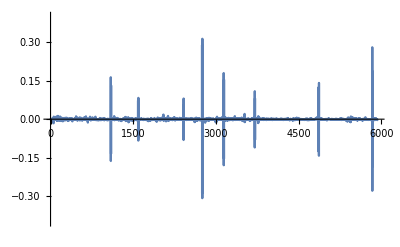

```mathematica
ListLinePlot[rsUniWeth90dFiltered, PlotRange->{-0.4, 0.4}]
```

```mathematica
(* Look at it in comparison to the 30d sampling for UNI/WETH ... *)
```

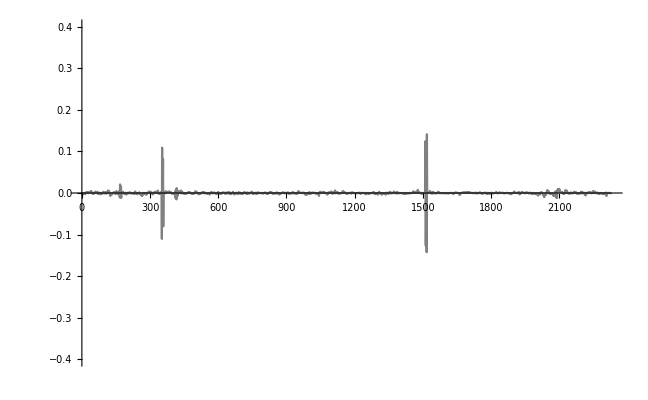

```mathematica
ListLinePlot[rsUniWeth, PlotRange->{-0.4, 0.4}, PlotStyle->Gray]
```

```mathematica
(* Note, the prior 30d sampling doesn't include the last few days at end of June, which had a large bump up. Included in the 90d pull (see ~ 6000 element). *)
```

```mathematica
(* Check again we're not normal ... *)
```

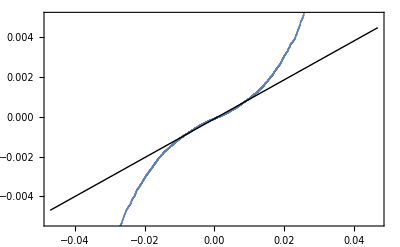

```mathematica
QuantilePlot[rsUniWeth90dFiltered]
```

```mathematica
(* Let's fit the 90d data ... *)
```

```mathematica
edistUniWeth90dFiltered = EstimatedDistribution[rsUniWeth90dFiltered, StableDistribution[1, aUW90d, bUW90d, locUW90d, scaleUW90d]]
```

StableDistribution[1,1.29905,0.00317474,-0.00011575,0.000868971]

```mathematica
(* And compare with prior 30d fit *)
```

```mathematica
edistUniWeth
```

StableDistribution[1,1.32783,0.0816836,-0.0000252748,0.000640944]

```mathematica
(* Actually, this isn't terribly different which is great. alpha estimation looks consistent at first glance for UNI/WETH *)
```

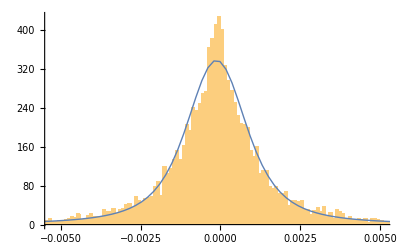

```mathematica
Show[Histogram[rsUniWeth90dFiltered, {0.0001}, "PDF"], Plot[PDF[edistUniWeth90dFiltered, x], {x, Min[rsUniWeth90dFiltered], Max[rsUniWeth90dFiltered]}, PlotRange->All, PlotStyle->Thick]]
```

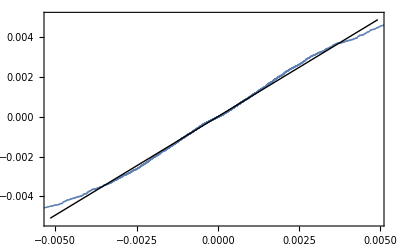

```mathematica
QuantilePlot[rsUniWeth90dFiltered, edistUniWeth90dFiltered]
```

```mathematica
(* hmm still slightly off at ends but not terrible *)
```

```mathematica
(* Compare the CDFs *)
```

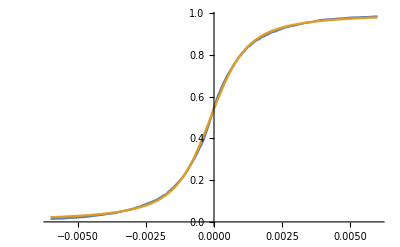

```mathematica
Plot[{CDF[EmpiricalDistribution[rsUniWeth90dFiltered],x],CDF[edistUniWeth90dFiltered,x]},{x,-0.006,0.006}]
```

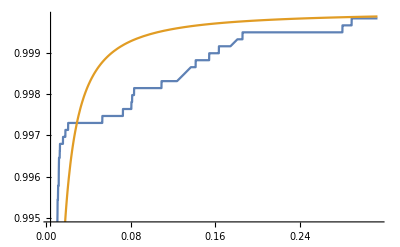

```mathematica
Plot[{CDF[EmpiricalDistribution[rsUniWeth90dFiltered],x],CDF[edistUniWeth90dFiltered,x]},{x,0.004,Max[rsUniWeth90dFiltered]}]
```

```mathematica
(* Nice ... *)
```

```mathematica
(* Filter out last month, so only analyzing first month of data *)
```

```mathematica
Length[tblUniWeth90d]/2
```

2976

```mathematica
tblUniWeth90d[[2976]]
```

{2975,1.62173×10^9,8.912×10^15}

```mathematica
FromUnixTime[tblUniWeth90d[[2]][[2]]]
```

Sun 18 Apr 2021 17:11:37GMT-4.

```mathematica
FromUnixTime[tblUniWeth90d[[2976]][[2]]]
```

Sat 22 May 2021 21:52:37GMT-4.

```mathematica
rsUniWeth90dFiltered1stMo = Table[rsUniWeth90dFiltered[[i]], {i, 1, 2976}]
```

{0.00192969,-0.000607667,-0.00173262,-0.000132253,-0.00086947,-0.000234575,0.00029493,0.000681779,-0.000561976,-0.0000244193,-0.000716273,-0.00281989,-0.0061241,-0.00436219,-0.0028575,-0.0016026,-0.00171996,-0.00208265,-0.00492299,-0.00466207,-0.00608829,-0.00613371,-0.00197327,-0.0024023,-0.00131026,0.000349446,-0.00141121,0.00143972,0.00305022,0.000848964,-0.000129127,-0.000101247,-0.00174334,-0.00524166,-0.00259329,-0.00437169,-0.000981283,0.000113154,0.000557693,0.0000323181,0.00200646,0.00113606,0.00086718,0.0014085,0.000177804,-0.000247883,-0.0014159,-0.00147833,-0.00154304,-0.00120511,-0.000743919,-0.00151442,-0.00624358,-0.0160456,-0.00169261,0.000861962,0.000509704,0.00145887,0.00985411,0.0021252,0.0018879,0.000373604,-0.000549284,-0.00159029,-0.00219189,-0.00119695,-0.000672857,-0.00213573,-0.000743938,-0.000477587,-0.00201632,-0.00158615,0.000858886,0.00112823,0.0032896,0.00324135,0.00123393,0.0022884,0.0014368,-0.000451669,0.000884978,0.000124196,-0.00207275,-0.00265967,-0.00128178,0.00143656,0.00321477,0.00409427,0.00757381,0.00359098,0.000750012,0.000268311,0.000524408,-0.000109422,-0.00220157,-0.00162811,-0.000864264,-0.00176446,-0.000167409,-0.000738056,-0.000366034,0.000351581,-0.00183872,-0.000627489,-0.0000928111,0.000255937,0.000160963,0.00289472,0.0106031,0.00277423,0.00198178,0.00141998,-0.00103407,-0.00100713,-0.00418503,-0.00551398,-0.00495665,-0.00609162,-0.00139984,-0.00343811,-0.00556887,-0.00319381,-0.00360722,-0.0013441,-0.000464528,0.000279331,0.00267327,0.00367708,0.00351294,0.00436995,0.00571279,0.00828066,0.0128565,0.0119613,0.00450544,0.00232584,0.00679721,0.00565367,0.00236304,0.00352364,0.00897462,-0.00133487,-0.00295649,-0.000945425,0.00118496,-0.000657976,0.0000943697,-0.00166117,-0.00201072,-0.00586238,-0.00220778,-0.00363562,-0.00269695,-0.000137415,-0.000502273,0.000075331,-0.00026691,-0.000758134,-0.000979879,-0.0017346,-0.0012714,-0.000355594,-0.00268786,-0.00506254,-0.00154902,-0.00107909,0.00160334,0.00251319,0.00697,0.00639826,0.00466253,0.0105968,0.00369881,0.00154319,-0.000549132,0.000823282,0.000895216,0.00446515,0.00500129,0.00695899,0.00407872,0.00309691,0.000681492,0.000913423,0.00258659,0.00286975,-0.000393521,0.00110135,-0.00310702,-0.00606018,-0.00717393,-0.00415347,-0.000672066,-0.00137831,-0.0000386547,0.000207469,-0.000254617,-0.000336538,0.000491034,0.00417185,0.00577956,0.00495891,0.0045621,0.000822076,0.00165217,0.000834761,0.00142728,0.00259822,-0.00112134,-0.00340925,-0.00573364,-0.0040864,-0.00450318,-0.0044657,-0.0010706,-0.00630258,-0.000821929,-0.000517005,-0.00105706,-0.000363876,-0.00268357,-0.00357889,-0.00844065,-0.00593022,-0.0016092,-0.00450008,-0.00149925,-0.000855666,-0.00214525,-0.000902781,-0.00133239,-0.00140195,-0.000524758,-0.00250277,-0.000589089,-0.00424938,-0.00684908,-0.00464391,-0.00294484,-0.000765677,-0.00203315,-0.000588344,0.000884908,-0.0000249737,0.000815021,0.00192178,0.000382254,0.00493564,0.00155319,0.000371111,0.000542473,0.00077627,0.000379193,8.42673×10^-7,0.00338729,0.00251186,0.00325071,0.00311472,0.00278859,0.00119444,0.000853803,0.00332291,0.00244411,0.000139995,-0.00111076,-0.00240553,-0.00415861,-0.00243837,-0.00116991,-5.12811×10^-6,0.000829103,-0.00259045,-0.000892033,-0.00335992,-0.0018707,-0.00212882,-0.00353118,-0.000754313,-0.000164094,0.00321398,0.00597179,0.0058837,0.00372305,0.00257138,0.00291342,0.00307068,0.000460192,-0.000833543,-0.00151877,-0.000912032,0.000954153,0.000271099,0.00204536,0.0011928,-0.000529638,-0.0000334055,0.000312518,0.00189333,0.00423103,0.00505428,-0.0000162221,-0.000249525,-0.00352585,-0.00229395,-0.00483072,-0.00441392,-0.00192689,-0.00336513,-0.00196128,-0.00233983,-0.00448962,-0.00065366,0.000599461,0.000446761,0.00156609,0.000242567,0.0000124432,-0.00389326,-0.00240327,-0.00324808,-0.00271756,-0.00385218,-0.00456073,-0.00166288,-0.000830699,0.000404722,0.000665508,0.000422272,-0.000471741,-0.00104512,-0.00252667,-0.00551587,-0.000519274,-0.0012443,-0.0000201565,0.000894692,0.00231379,0.00169548,0.00138337,0.000467412,0.000815413,0.00027029,0.00260654,0.00102001,0.00168291,0.00365333,0.00207123,-0.00294048,-0.0010807,-0.00307204,-0.00327139,-0.00160102,-0.00260264,-0.00199442,-0.000690494,0.000712734,0.000563387,0.000632592,0.00250654,0.00182425,0.0012268,0.00177874,0.000711835,0.000799131,0.000341433,0.000189725,-0.00037428,-0.000501512,-0.00085063,-0.00148635,-0.000375853,0.00165052,0.003238,0.00103432,0.00215819,0.00121866,0.000684921,-0.000852468,0.0000349074,0.00020368,0.000262281,0.0000876259,0.000853762,0.000770367,0.00114369,0.000313132,0.000130765,-0.000684331,-0.000146966,-0.000156594,0.0026363,0.000753676,0.00182103,0.000312798,-0.00135665,-0.00853066,-0.00213096,-0.00310008,-0.00134899,-0.00308489,-0.000179669,-0.000562142,-0.00290801,-0.000342354,-0.000158294,-0.00122259,-0.00198498,-0.00119043,-0.00140946,-0.00111369,-0.00154334,0.000123918,0.000371351,0.0000553607,-0.000183641,-0.000555279,-0.00229761,-0.00248606,-0.00139014,-0.0000745267,-0.0000419324,-0.0000867336,-0.0000224396,0.000852751,0.000539613,0.000308568,0.000797852,0.000992912,0.000235007,-0.0000670733,-0.000125186,0.000323915,0.00226718,0.000371173,0.000587002,0.0024282,0.000543501,0.000997984,0.00045313,0.000134421,0.00138367,0.000165694,0.00191153,0.00196392,0.000450352,0.000888912,0.000731973,0.000445911,-0.000169493,0.00008817,-0.000131413,0.00017345,0.000206272,0.000166004,-0.000189359,-0.0018377,-0.000593888,-0.000590728,0.000340829,0.00321526,0.00676279,0.00850133,0.01118,0.00776528,0.0053995,0.00287906,0.00321254,-0.000918207,-0.000643793,0.000649187,-0.000645721,0.000637558,0.00143186,0.000233684,-0.00178226,0.000764462,0.001569,0.00205761,0.00427191,0.00682733,0.003415,0.00171875,-0.000618249,-0.00136712,-0.00494985,-0.00291967,-0.00315682,-0.00427202,-0.00293189,0.00407563,0.00162927,0.00235365,0.00172372,0.00193912,-0.0000874736,-0.000911629,-0.000533103,0.0000273406,-0.00285645,-0.00191121,-0.00400741,-0.00351907,-0.00294886,-0.0032603,0.00175622,0.00401155,0.00074853,0.000876379,0.00216939,0.0000398306,0.000476983,-0.000571405,-0.000312685,-0.000109395,-0.000452529,-0.00159577,-0.00157895,-0.000567104,0.000521195,0.00111387,0.00110617,0.00203436,0.00173102,0.00271089,0.00393858,0.00289535,0.00713715,0.00202708,-0.000809828,-0.00253161,-0.00216931,-0.00407574,-0.00180948,-0.00109866,-0.00455076,-0.00174192,-0.00244699,-0.00219375,-0.00311828,-0.000919075,-2.34019×10^-6,-0.000971333,-0.00248715,-0.000459318,-0.00124792,0.000268929,0.00125824,0.00262696,0.00505987,0.00573864,0.00300649,0.00292918,-0.000051636,-0.00227166,-0.00256193,-0.00185387,-0.000979611,-0.000910351,-0.000700557,-0.000203627,-0.000215146,-0.000339977,-0.000411542,-0.000589392,-0.00105309,0.00262468,0.00128801,0.00122281,0.0017582,0.000900432,-0.00191299,-0.0020612,-0.00216632,-0.00620552,-0.0045409,-0.00343158,-0.00112282,-0.0000663407,0.000178542,0.00062904,0.00164214,0.000872426,0.000824965,-0.000046278,-0.000248683,-0.000455618,-0.000258472,-0.00138604,-0.00161512,-0.00169831,-0.00101443,-0.000928836,-0.00108869,0.0000394136,0.00077356,0.00126544,0.00203559,0.00353315,0.00279978,0.00159835,0.00195018,0.00105639,0.00326891,0.00111495,0.000479338,0.000653829,0.000738997,0.00181723,0.00438017,0.00582612,0.00716808,0.00598134,0.00191072,0.00387426,0.00248223,0.00334952,0.00139541,0.000443106,0.000286274,-0.000104894,-0.00196205,-0.0021153,-0.00152851,-0.000635183,0.0000888164,0.000453118,0.000941904,0.000313166,0.00102578,-0.000138638,-0.000308702,-0.00251402,-0.00108242,0.00132205,0.00629402,0.000681594,0.00370245,0.00140382,0.0012934,0.00370748,0.00234977,0.0110172,0.00960656,0.00607852,0.00243116,0.000733926,0.00015669,-0.000489736,-0.0016928,-0.00165371,-0.0019965,-0.00351981,-0.00165857,-0.0010329,-0.000727654,0.000936958,0.00222003,0.00100714,0.000311399,-0.000046139,0.000884252,0.00200603,0.00228046,0.00113778,0.00167268,-0.000422343,-0.0032559,-0.00452348,-0.00344922,-0.00164639,-0.00104203,-0.00505185,-0.00149032,-0.00122292,-0.00228987,-0.000709954,-0.0132099,-0.00472336,-0.00289845,-0.00442952,-0.00299415,-0.000668873,-0.000640838,0.0000446586,-0.000230795,0.00111819,-0.00313463,-0.00112047,-0.00124734,-0.00137935,0.000196703,0.000954082,0.000830524,0.000890808,0.000677159,0.00110263,0.000727174,0.00124557,0.000088296,0.00013582,0.00131065,0.000354392,0.000517074,0.000917703,0.00141381,0.000380272,-0.000370609,-4.63973×10^-6,-0.000817374,-0.00248197,0.000319979,0.0013295,0.00385287,0.00517742,0.00852067,0.00962261,0.00296011,0.000831913,0.000388973,-0.00158708,-0.00146472,-0.000971457,-0.00114867,-0.00146751,-0.00157611,-0.000951051,-0.00364018,-0.00109553,-0.00379601,-0.000976114,-0.00119811,-0.000133164,-0.000429145,0.000213347,-0.00446918,-0.00301936,-0.0017431,-0.00291887,-0.00158933,-0.00256249,-0.00206119,0.000965876,0.00147684,0.00225284,0.00542484,0.00155055,0.00176175,0.00232864,0.000838765,0.00137677,-0.000431069,-0.000412108,-0.00225773,-0.00016225,0.000558463,0.000389505,0.000115146,-0.000378475,0.000393791,0.00140168,0.00172255,0.00124948,0.00667202,0.00131253,0.00489851,0.00204553,0.00176138,0.0044044,0.000513057,-0.000332628,-0.000550753,0.00131916,0.0027429,0.000639411,-0.000465314,0.000548037,-0.000484813,-0.00204468,-0.00172056,0.00206128,0.00301443,0.00126338,0.00302802,0.000381349,0.000265874,0.000408594,-0.000751893,-0.00303044,-0.000536573,-0.000462933,-0.000322778,-0.000662855,-0.0025626,-0.000371803,-0.000958164,-0.00075012,-0.00106176,0.000368962,-0.00107988,-0.00133012,-0.00122396,-0.0000514923,-0.000573313,-0.00102527,-0.000873758,-0.000145148,-0.000741708,0.0000209018,0.00141572,0.00201562,0.00176439,0.0047878,0.00380883,0.00966689,0.00186132,0.00358629,0.00114359,-0.00239811,-0.00348996,0.00100086,0.00171804,0.00170355,0.00303241,0.00105777,-0.000415846,-0.000607121,-0.000849616,-0.00093026,-0.00256657,-0.00241845,-0.00224555,-0.0020303,-0.00068259,-0.00136722,0.000126993,0.0000103824,0.000684621,0.000403279,0.00052913,-0.000608088,-0.000498413,-0.00219799,-0.00183698,-0.00454816,-0.00256398,-0.00110702,-0.000847941,-0.000149673,-0.000205801,-0.0000237435,-0.000633298,-0.000195794,-0.0012874,-0.000550924,-0.00139171,-0.000846325,-0.00171063,-0.00360869,-0.00107964,-0.000703913,0.0000456927,0.0000387081,0.0000632306,-0.00064244,-0.0011292,-0.00239168,-0.00226257,-0.00353482,-0.00200177,-0.000256632,-0.000143045,-0.00099106,-0.00278607,-0.00085163,-0.00442305,-0.000927906,-0.0017131,-0.00139785,-0.000721338,-0.00204527,-0.00148348,-0.00360023,-0.00281543,-0.000627456,-0.000618139,0.000317757,0.00226881,0.000869291,0.000492031,0.00112252,0.00115689,0.000474833,0.00196063,0.00211097,0.00135246,0.00480095,0.000808245,0.00257659,0.000663288,-0.000218564,-0.000398648,0.000118278,0.0000256638,-0.000121649,-0.000177662,-0.000339908,-0.00135692,-0.000908175,-0.000464375,-0.00105728,-0.000875057,-0.00295222,-0.00313469,-0.00423573,-0.00163434,-0.00017761,-0.000677144,-0.00115828,-0.00259735,-0.000848908,-0.000676098,-0.00108945,-0.000489878,-0.000982049,0.00169944,0.000713208,0.000517026,-0.0000923344,-0.000350444,-0.000896356,-0.00061308,-0.000304056,0.000590796,0.00238155,0.00299106,0.00140752,0.000695577,0.00117596,-0.000495767,-0.00146131,-0.0026809,-0.000603176,-0.000240786,0.00044433,0.000394681,0.000457607,0.000361333,0.00007433,0.000242381,0.0000685217,-0.000319771,-0.000218422,-0.00086033,-0.00178433,-0.0016967,-0.00143803,-0.000916302,-0.000975632,-0.000792806,-0.000932112,-0.000688369,-0.000426979,0.000846077,0.0015105,0.00374784,-0.000268038,-0.0000526922,-0.00175554,-0.00173961,-0.00170839,-0.00349906,-0.00233896,-0.00263031,-0.0044165,0.000895785,0.000445821,0.00440251,0.00268197,0.00190073,0.00164146,0.000451719,0.000546788,-0.000288863,-0.000204343,0.00141084,0.000339061,0.000520318,0.00101531,0.000512606,-0.000293133,-0.000158365,0.0000670551,-0.000452494,-0.00045201,-0.000404548,-0.000132407,-0.000252673,-0.000271179,-0.000409177,-0.000351398,0.000902858,0.0000360546,-0.00049041,0.0001713,0.0000996773,-0.000677741,0.000147653,0.000530889,-0.000169485,-0.000295015,-0.000440138,-0.00125089,-0.00198459,-0.00164623,-0.00186409,-0.00304597,-0.00374977,6.3804×10^-6,0.000147091,0.00020863,0.000610496,0.000947067,-0.000317958,-0.000612438,-0.000395213,-0.000724279,-0.00224463,-0.000650167,-0.000391266,-0.000975343,-0.000854556,-0.00126483,-0.00142126,-0.00148335,-0.00399475,-0.000412067,-0.000194583,0.000812175,0.00186319,0.000337305,-0.00223041,-0.00109128,-0.00447834,-0.00399988,-0.000385845,-0.00136221,-0.000639065,-0.00230437,-0.000617205,-0.000328268,-0.00016768,-0.00103031,-0.000466909,-0.0000679272,-0.00140513,-0.000575677,-2.04493×10^-6,0.000049849,0.000294166,0.00112606,0.000727205,0.000042649,-0.000341417,-0.000667444,-0.00085112,-0.000200836,-0.000511178,-0.00134996,-0.00128897,-0.00160836,-0.00233703,-0.00170276,-0.000390854,-0.000735509,0.000272109,-0.000435444,-0.000619131,-0.000643301,-0.00252692,-0.00314314,-0.00102223,-0.000345941,-0.000638363,0.000842642,0.000722372,0.000069089,-0.000549723,-0.000434852,-0.0016987,-0.000573309,-0.000338577,0.000817324,0.163244,-0.162777,-0.000518543,-0.000884996,-0.00177701,-0.134707,0.131443,-0.00197418,-0.000491607,-0.0000640774,0.0000814673,0.000261378,0.00060643,0.000670359,0.00105743,0.0000772625,0.000660057,0.000172064,-0.000221283,0.000599693,0.000521226,0.000189335,0.000657577,0.000941767,-0.000231772,-0.0000998942,-0.000170076,-0.000161386,-0.000221784,-0.000118839,-0.0000941378,-0.000132884,0.000578227,0.00210725,0.00110669,0.000288413,0.000240157,0.0000502246,-0.000185199,0.000316408,0.000294451,0.000881493,0.000351473,0.000618623,0.000194992,0.00013219,-0.000363037,0.000214636,0.00101979,0.000651698,0.00206687,0.00306172,0.00267517,0.00379017,0.00169046,0.00250869,0.00156492,-0.000193159,-0.000963573,0.00255157,0.00583518,0.00635902,0.0118816,0.00742998,0.00776283,0.00317544,-0.000700249,-0.00422265,-0.00156013,-0.00190114,-0.00275221,-0.000936415,0.000848008,0.000416774,0.00081702,0.00186851,0.0024201,0.00115155,-0.000870807,0.0000614322,-0.00177616,-0.00138693,-0.000371618,-0.000863518,-8.69914×10^-6,5.9366×10^-6,-0.000143014,-0.0000591058,-0.000465135,-0.000764835,0.000346647,0.000375505,0.0000673913,0.000658899,0.000757001,-0.0012408,-0.000577619,0.0000377829,-0.000584528,-0.000372454,-0.000544171,-0.000662002,-0.00267365,-0.000862699,-0.0015992,-0.00102638,0.000373378,0.000410553,0.00118183,0.00153157,0.00132015,0.00182586,0.000740538,0.00159674,-0.00264363,-0.000585172,-0.0018727,-0.000524599,0.00012643,0.000911819,0.00224632,0.00494865,0.00253873,0.00348869,0.00201242,0.00128659,-0.0010907,-0.000383729,0.000339067,0.000889613,0.000735845,0.00125993,0.000616174,-0.000618187,-0.00155091,-0.00201942,-0.00302566,-0.00407987,-0.00165289,-0.00177477,-0.000813244,-0.0018172,-0.0016855,-0.00134227,-0.00229156,-0.00323094,-0.00215639,-0.00318261,-0.0031905,-0.00145518,-0.00512848,-0.00320559,-0.0028137,-0.00165378,-0.00150626,-0.000995549,-0.00255633,-0.000448522,-0.0004009,-0.000245855,0.0000405849,0.000932265,0.000592786,-0.000304097,-0.000331394,-0.00170983,-0.00161446,-0.0018712,0.000153192,0.000508552,0.00146412,-0.000178008,-0.00174924,-0.00314661,-0.00187499,-0.00164855,-0.000731986,-0.00103752,-0.00236433,-0.00104466,-0.00243702,-0.00146858,-0.00136228,-0.00194647,-0.00698363,-0.0046579,-0.0065464,-0.00627241,-0.00233759,-0.00628939,-0.00147857,-0.00273169,-0.0031558,-0.0074111,-0.00521956,-0.0046407,-0.00154655,-0.000422195,-0.000817992,-0.00212262,-0.00136664,-0.00235066,-0.00316021,-0.0010371,-0.000726028,-0.00135601,-0.00208775,-0.00172024,-0.00374334,-0.00280321,-0.00302188,-0.00109098,-0.00228911,-0.000900081,-0.000608792,-0.00108072,0.00100984,-0.000761129,-0.0000200713,0.000262338,0.00041039,-0.000795377,0.000243376,0.00188933,0.000865308,0.00138259,0.00186455,0.00115785,0.0022266,0.000684502,0.00095376,0.00164078,-0.000163915,-0.00174798,-0.00114177,-0.00130626,-0.00174374,-0.00191273,-0.000799819,-0.000404458,-0.000666307,-0.000694693,-0.000884312,0.000119306,0.000159061,-0.000364131,-0.000389649,0.000132374,0.000672638,0.000517062,0.00139656,0.00245821,0.000138267,-0.000189088,-0.000185768,-0.000230975,-0.000110617,-0.000571078,-0.00163162,-0.00170004,-0.00211298,-0.002116,-0.00365967,-0.00167336,0.00584319,0.00799115,0.00577614,0.00885554,0.0088055,0.000546233,-0.00294687,-0.00286264,-0.00733386,-0.00390497,-0.00509513,-0.00634412,-0.0021258,-0.00111805,0.000936836,0.00454161,0.00492472,0.00240353,0.001092,0.000512948,0.00171468,0.00174525,0.00236239,0.000815642,0.000401408,0.000935198,0.000724225,0.00022956,0.00178094,-0.000123732,0.000408404,0.00112469,0.000969815,-0.000603827,0.000393988,-0.000120391,-0.000195862,-0.00113693,0.000249145,0.00244401,0.00353156,0.00433332,0.00377563,0.00482286,0.00479654,0.00339897,0.00291304,0.00342888,0.00145959,0.00314477,0.00206912,0.000913319,0.00755408,0.00308206,0.00327046,0.00247437,-0.000128127,-0.00626219,-0.00953504,-0.0121901,-0.00537988,-0.00937274,-0.00333764,0.00477328,0.00349915,0.00245697,0.00235357,0.000755299,0.00175412,0.000412104,0.000204713,0.00108685,0.000992557,0.000793834,0.000835508,-0.000262922,-0.000660585,-0.00137079,-0.00080671,-0.000260565,0.000615783,0.000681825,0.00132818,0.00140564,0.000444362,0.000361662,0.00107679,0.000312342,0.00147904,0.00155041,0.0011498,0.00144602,-0.00199022,-0.000848219,-0.00527934,-0.00250285,-0.00252398,-0.000702885,-0.00170832,-0.00045035,0.000226566,-0.000512576,0.000520667,0.00157987,-0.00141628,-0.00149137,-0.000703481,-0.00175709,-0.000987474,-0.000997456,-0.00166145,-0.00152326,-0.000640134,0.0000339262,0.00174707,0.00446002,0.00296702,0.00201411,0.000779442,0.000856735,0.000250805,-0.000284272,-0.000309293,-0.00146966,-0.00309204,-0.00607031,-0.0055389,-0.00476187,-0.00537884,-0.0038632,-0.00394112,-0.00162335,-0.0000484105,0.000594087,0.000791886,0.00102149,0.00346601,0.00230086,-0.00196885,-0.00106352,-0.00289981,-0.0062504,-0.00385629,-0.00227424,-0.000866927,-0.00105945,-0.00101811,-0.000530035,-0.00277558,-0.00187078,-0.00138811,-0.00236442,-0.00116409,-0.00106719,-0.00245096,-0.00204081,-0.00487081,-0.00124477,-0.0022924,-0.00404868,-0.00128418,-0.00115071,-0.000927433,-0.000531421,9.43646×10^-6,-0.0000773662,0.000368214,0.00040704,-0.000221111,-0.000120944,-0.000215558,-0.000429147,-0.00044289,-0.000241166,-0.000176669,-0.000106309,0.00010756,0.00102966,0.00296756,0.00139416,0.00159913,0.000671677,0.000543826,0.0000984226,0.000570682,-0.000108324,-0.000213955,0.000304349,0.00263048,0.000466632,0.00137635,0.00118382,0.000784576,0.000445576,-0.00267304,-0.00110018,-0.00172413,-0.000750583,0.00018081,0.000147489,0.0024773,0.00176471,0.0011275,-0.000141125,-9.20875×10^-6,-0.00138015,-0.0041645,-0.00199919,-0.00157754,-0.00139742,-0.00197267,-0.00286627,-0.00126085,-0.00122245,-0.000754101,-0.000403699,-0.000422298,-0.000067497,-0.000407271,-0.000539008,-0.00119158,-0.000857198,-0.000798325,-0.00125359,-0.00232364,-0.000453692,-0.00369574,-0.00443735,-0.00417816,-0.00316901,-0.000747895,0.0724397,-0.0734371,-0.00040365,0.000705977,0.000232064,-0.0834354,0.0830013,-3.39462×10^-6,-0.000392987,0.00181262,-0.0000534637,-0.0000585054,-0.000136491,0.000221741,-0.000815369,-0.000211127,0.000201114,0.000919556,0.000389107,-0.000197732,-0.000577232,-0.000441822,-0.00210863,-0.00225163,-0.00122345,-0.000735656,-0.000140838,-0.00197044,-0.00233451,-0.000931029,-0.00175648,-0.00107885,-0.00234165,-0.00136519,-0.000388793,-0.000310806,0.000306843,0.000442897,0.000377822,0.000399022,-0.000564702,-0.000269287,-0.0000657028,-0.0012819,-0.000899849,-0.00254351,-0.000878736,-0.000693075,0.000421702,0.000614085,0.00111243,0.000784995,0.00222725,0.00107728,0.000876644,0.000622808,0.000613805,0.00134503,0.00090878,0.00131931,0.00203706,0.00104587,0.00240497,0.00255248,0.00210389,0.00187164,0.000458426,0.000805639,0.000834477,0.0000234076,3.05261×10^-6,0.000280694,0.000102689,-0.000191309,-0.000414238,0.000157347,-0.000197309,0.000551643,0.000773783,0.0013233,0.000034478,-0.000217487,-0.000212025,-0.000178425,-0.000359437,-0.0000801826,-0.000251056,-0.000512491,0.000106277,-0.0000710692,-0.0000243105,-0.000306447,-5.512×10^-6,-0.00190162,-0.00232052,-0.00090076,-0.00145433,-0.0023871,-0.00288527,-0.00358085,-0.00211927,-0.00145052,0.000299268,0.00150864,0.00241341,0.00129805,0.000642827,-0.0000526461,-0.000124826,-0.00123402,-0.00124128,-0.00095521,-0.00206392,-0.000565113,-0.000318052,-0.000365437,0.00031337,0.000312109,0.000126904,-0.0000852168,-0.000574598,-0.00118401,-0.00160946,-0.00278385,-0.00182108,-0.000948401,-0.00025973,0.00084216,0.000640432,-0.000129688,-0.000436843,-0.00012541,-0.00239933,-0.000541537,-0.000878659,0.000063025,0.00060722,0.000729414,0.000655247,0.000894404,0.000754202,0.000443526,-0.000158278,-0.00054184,-0.000732051,-0.000556931,-0.000954483,-0.000385994,-0.00113362,-0.000794143,-0.000656491,-0.00122963,-0.000152403,-0.004121,-0.000928589,-0.000586902,-0.00028869,-0.00018074,0.0000587793,0.00189636,0.001476,0.000309499,0.0000810006,0.00043499,-0.000628643,0.0000716128,0.0000481573,0.0000171382,-0.000469366,-0.000802884,-0.00159778,-0.00116148,-0.00376148,-0.00434794,-0.0045577,-0.00236409,-0.00374953,-0.00164793,-0.000971846,0.0000747037,0.00111498,0.00222801,0.00247448,-0.00169948,-0.0053174,-0.00462007,-0.00791304,-0.00295151,-0.0027465,-0.0033182,-0.000608938,-0.000888663,0.000236523,-0.000259154,-0.000604651,-0.000453661,-0.00306556,-0.00254685,-0.00216252,-0.00517168,-0.00118205,-0.00536251,-0.00410774,-0.00266459,-0.000200488,0.000182167,-0.00154682,-0.000861936,0.00036706,0.000328557,0.000264441,0.00116397,0.00029797,-0.000107882,-0.000985376,-0.000611745,-0.00066723,-0.000520812,-0.00174828,-0.00244869,-0.00404673,-0.00265425,-0.00642101,-0.0023073,-0.0015804,-0.00187456,-0.00442182,-0.0037066,-0.000851279,-0.000632709,-0.00114897,-0.000833974,-0.00118551,-0.00338776,-0.000390865,0.00142311,0.00125462,0.00294315,0.00142504,0.00184253,0.000880243,0.00436265,0.00152346,0.000594239,0.000760162,0.000357958,-6.8064×10^-6,-0.000468534,-0.000272261,-0.000582585,-0.0000335833,0.00134484,0.000619045,0.000605218,0.000874809,0.000155379,0.000120705,0.000168495,0.000222267,-0.000100988,0.0000110017,-8.69603×10^-6,-0.000218028,-0.000175512,-0.0000730761,-0.00047753,-0.00107435,-0.00340905,-0.00318255,-0.00251379,-0.00265175,-0.000547987,-0.000912324,0.000363332,0.000558173,-0.0000766971,-0.0000659023,-0.0000602884,-0.000225518,-0.000056277,-0.000210862,-0.000288761,-0.0000831954,-0.000128455,0.000377669,0.000181892,0.000239579,0.000640134,0.0000120246,-0.000316511,-0.000184668,0.0014285,0.00137313,0.000325024,0.000810839,0.0015465,0.000343863,0.00051855,0.00163618,0.00458778,0.00123335,0.000581098,0.000702456,0.000397316,-0.00101071,-0.000496607,-0.0019429,-0.002493,-0.000849873,-0.0014929,-0.000346854,-0.00113713,-0.00229002,-0.000860888,-0.00444151,-0.00189055,-0.00135798,-0.00382574,-0.00155773,-0.00137358,-0.000779633,-0.000458743,-0.000763556,-0.00263875,-0.00470895,-0.00162398,-0.00288059,-0.000468649,-0.000954063,-0.00285876,0.000140842,0.0011878,0.000627421,0.000493032,0.000909981,-0.0014852,-0.00210477,-0.00731561,-0.0104705,-0.00129389,-0.00202102,-0.000584836,-0.00157754,0.0000635975,-0.000359919,0.000102837,-0.00368292,-0.00216979,-0.00339949,-0.00534335,-0.00413897,-0.00375224,-0.00223543,-0.00331557,-0.00520527,-0.00475385,-0.000954626,0.00662461,0.00493215,0.000787318,0.00134305,-0.0000340621,-0.000335341,-0.00174689,-0.00113484,-0.00198668,-0.00136757,-0.00144537,0.000239136,0.000227285,0.000157313,0.000604955,0.000740498,0.000660008,0.000427215,0.00191418,0.00207738,0.00307054,0.00180743,0.00259327,0.00161257,-0.000392691,-0.000329075,-0.000229021,-0.000194571,0.000468333,0.00186235,0.000807129,0.00125574,-0.00408344,-0.00123929,-0.00144387,-0.000611609,-0.000196336,0.000404984,0.000699154,0.000962015,0.000517783,0.000715181,0.00216594,0.000663668,0.000823851,-0.00150624,-0.000699806,-0.00144449,-0.00538809,-0.00246828,-0.00192825,0.00185958,0.000691732,0.0018427,0.000553136,0.00145691,0.000339662,0.000111562,-0.00130547,-0.000712053,-0.00110626,-0.00281143,-0.000872964,-0.000196408,-0.0000322342,-0.000127936,0.0014703,-0.000965894,-0.000558131,-0.000442943,-0.000320733,-0.00343279,0.000246927,0.000789643,-0.00083172,-0.00102438,0.000896633,0.000192865,0.00105095,0.00159276,0.0019765,0.00367691,0.000296276,0.00370859,0.00362795,0.00168859,-0.000422828,-0.0014681,-0.00191649,0.000323875,0.00403222,0.00588381,0.00714856,0.0104981,0.000558999,-0.00303753,-0.00332619,-0.00126522,-0.000964799,0.00185876,0.00461572,0.00985215,0.01039,0.0180045,0.00849946,-0.00155216,-0.0000867857,-0.00274569,-0.000819545,-0.00123304,-0.00680459,-0.00143885,-0.00323822,-0.0028203,-0.0022198,-0.00265183,0.00284903,0.0010309,0.001258,0.00167002,0.00105112,-0.00161347,0.000737174,-0.000171423,-0.000837759,-0.0000979213,0.000705114,-0.000481815,0.00249223,0.0029343,0.00346847,0.00288573,0.00318507,0.00210082,-0.00084428,-0.000777904,-0.000746802,0.000490547,0.000588332,0.000247905,-0.000317987,0.000383928,-0.00132866,0.000288281,0.00109325,0.0000485966,-0.00188845,-0.00100342,-0.00318056,-0.00252963,-0.0035289,-0.00863397,-0.00385608,-0.00627925,-0.00360247,-0.00216938,-0.000727134,-0.000777032,0.00137975,0.00173923,0.000777194,0.000876048,0.000188893,-0.000962686,0.00173614,0.0012268,0.000957909,0.00144448,0.00368054,0.00598088,0.0031543,0.00520922,0.0010918,0.00122803,0.00260614,0.000549345,-0.000127015,0.00014326,0.00077359,-0.0007436,-0.00179535,-0.00149051,-0.000748439,0.00107449,0.00128074,0.00614522,0.00714039,0.0126462,0.00666312,0.000518442,0.00059819,-0.0010877,-0.00202587,-0.00364301,-0.00603803,-0.0044872,-0.00684389,-0.00304798,-0.00138315,-0.00291222,-0.00192751,-0.00283196,-0.00171548,-0.00119402,-0.00132126,-0.000571819,0.0030382,0.0015171,0.00208464,0.000426948,0.000334556,-0.000758229,-0.000304548,-0.00161039,0.000205693,-0.000179561,0.000131535,0.00130744,0.00160275,-0.0000459715,0.00166229,0.00133726,0.000237238,6.74292×10^-6,0.000350733,0.000689133,-0.00207432,-0.00159679,-0.000798347,-0.00170032,-0.000104032,-0.00107835,0.000623984,0.000822151,0.000662314,0.0000731533,0.0037951,0.00244016,0.000827932,-0.000359272,-0.00059303,-0.000185532,-0.000505126,-0.000163536,-0.000721685,-0.000268081,-0.000947013,-0.000798937,0.000307918,0.000686428,0.00153718,-0.000352285,0.000216218,-0.000484763,-0.0000776125,-0.000528851,-0.000941785,-0.00131154,-0.00239409,-0.000978203,-0.00213981,-0.00194404,-0.000772624,-0.00108705,-0.00153631,-0.00183055,-0.00398307,-0.00170814,-0.00274631,-0.00155433,0.000211684,0.00105028,0.000917253,0.00150447,0.00435285,0.00143785,0.0000525969,-0.000540921,-0.000604626,-0.00068845,-0.0010743,-0.000088779,-0.000218739,-0.000450546,-0.0000442101,-0.0000105694,0.0000928295,8.58058×10^-6,0.00071445,0.000849281,0.00123682,0.00165729,0.00169389,0.00212129,0.00257405,0.00226659,0.00103378,0.0021795,0.00238265,0.00683425,0.00527525,0.00783464,0.00191065,0.00341497,0.00474873,0.00173439,0.00570518,0.000834272,-0.00173752,-0.00234965,-0.000421399,-0.00125774,-0.000726078,-0.00206166,-0.0042552,-0.00157518,-0.00464736,-0.00243094,-0.00140743,-0.000873985,-0.000563396,4.73686×10^-6,-0.0000364532,-0.000219822,-0.000145598,-0.000257826,-0.000840698,-0.000072379,-0.000816511,-0.000684989,-0.00108831,-0.00209802,-0.000539223,-0.00284534,-0.000507582,-0.000966293,-0.00138023,-0.000315607,-0.000329273,-0.000391293,0.0000814474,0.00040411,0.00149623,0.000901571,0.00141277,0.00342107,0.00383359,0.00162627,-0.000914455,-0.000431094,-0.000397053,-0.000684702,-0.000316315,-0.000569621,-0.00121308,-0.0017954,-0.000841059,-0.000769117,-0.000326314,-0.00063975,-0.00146472,-0.00113126,-0.00032685,-0.0026431,0.000453389,0.00205463,0.000731868,0.0000132955,0.00137856,-0.0000158033,-0.00153869,-0.000116585,-0.000148951,-0.00214567,-0.00181955,-0.000544543,-0.00152101,-0.0000576279,-0.000105133,0.000170306,0.000166808,0.000848309,0.000794013,0.000869864,0.00112708,0.000284886,-0.00067748,-0.000651456,-0.000763583,-0.0000491795,0.000147254,0.000596015,-0.000242084,-0.00025335,-0.000102726,0.000953087,0.0023664,0.00281625,0.0032847,0.00534271,0.00324466,0.00160122,0.00157414,0.00255546,0.000603179,0.00036587,0.00151602,0.000398853,-0.000527042,-0.000654294,0.000180746,-0.000784788,-0.00117191,0.000455991,0.000447588,-0.000584612,0.000501776,0.00118198,0.000947208,0.000895591,0.000754848,0.00113685,-0.00125453,-0.00203826,-0.00126309,-0.00075094,-0.00104203,-0.00182478,0.000257319,0.000845263,0.00183154,0.00112435,0.00271105,0.000532202,0.000412715,-0.000346511,-0.00117105,-0.00236012,0.0008359,0.000192165,0.000783373,0.00264794,-0.00104627,0.000413614,0.00155195,0.00173216,0.00124552,0.00153046,0.000647937,0.0000396357,-0.000374701,-0.00143845,-0.000402891,-0.00361091,-0.00157194,-0.000906173,-0.00139198,0.000460728,0.000277048,0.0000947452,0.000091789,-0.000596337,-0.0011621,0.000107758,0.0529326,-0.0521726,0.000604119,0.000299092,0.00043532,-0.0810712,0.0804054,-0.000787158,-0.00141192,-0.000360668,-0.000202577,0.0000257507,-0.0000228691,-0.000672354,-0.00118885,-0.00132985,-0.00128722,-0.000875944,-2.57906×10^-6,0.000454484,0.000336207,0.000555458,-0.000247309,-0.000653827,-0.0027898,-0.0026339,-0.00111504,-0.000589371,-0.0010794,-0.000441203,-0.00148793,-0.000770235,-0.0017003,-0.00121386,0.0000173989,0.00084009,0.000443368,0.00152583,0.0014945,0.00109944,0.00174409,0.00102331,0.000636745,0.000257716,0.000499746,0.000234604,0.00122408,0.000840995,0.000730489,0.00158261,0.000729354,0.000702549,0.000506823,-9.43505×10^-6,-0.000880877,-0.000669252,0.0000401906,0.00185163,0.0000195159,0.000944575,-0.00143363,-0.000509749,-0.00353111,-0.000372733,-0.000326162,-0.00134574,0.00135131,0.00105655,0.000734301,0.000156444,-0.000920554,-0.00052497,0.000549491,0.00178334,0.00173699,0.00236451,0.000663251,0.000160683,-0.000408172,-0.0014144,-0.00134121,-0.00110652,-0.000225445,-0.000203457,0.000774974,0.00115039,0.00141319,0.000716649,0.000690153,0.000398676,0.0000542673,-0.0000548553,-0.00048712,-0.00170305,-0.00147946,-0.00107224,0.000288005,-0.0000328604,0.000471147,0.000875915,0.0011009,0.00125608,0.00303075,0.00225716,0.0020281,-0.00016521,-0.000196012,-0.00025241,-0.000463211,0.000831142,0.000566557,0.000352479,0.000750185,0.00105954,-0.00128231,-0.000201552,-0.000286942,0.000123519,0.000138741,-0.000208447,-0.000309422,-0.000554375,-0.00202271,-0.00162252,-0.000150213,0.000630817,0.00110265,0.000137966,0.000868457,0.000742732,0.000522833,-9.58561×10^-7,0.00249279,0.00157077,0.00207033,0.00196523,-0.000395935,-0.000370225,-0.000905363,-0.000784062,-0.0000865089,-0.000126848,0.0000566822,-0.00136088,-0.00201679,-0.000938693,-0.00267537,-0.00077702,0.0000259564,0.00275856,0.00211954,0.00459173,0.0013168,0.000615836,0.000351204,0.000361564,-0.000189203,-0.0000871468,-0.000322357,-0.000433846,-0.000861234,0.000253949,-0.000234062,0.00026872,0.000353299,-1.5179×10^-6,-0.00154033,-0.00122965,-0.00157196,-0.000735475,-0.000660146,-0.00291314,-0.000359778,0.00107346,0.00155898,-0.000672626,0.000919793,0.00121817,-0.000485645,-0.00273334,-0.00265717,-0.000685699,-0.00104964,-0.00102898,0.00100998,0.000724561,0.000249725,0.000723278,-0.000281893,-0.0000970753,-0.0000284914,-0.000061478,-0.000850642,0.000259221,0.000103719,0.000154918,0.000217806,0.00238605,0.0002044,-0.00268041,-0.0047171,-0.00460529,-0.00462477,-0.00964498,-0.000904916,0.000205929,-0.000831385,-0.00488919,-0.0115052,-0.00876865,-0.0104284,-0.00280906,-0.00356458,-0.00403262,-0.00209469,0.000319198,0.000410653,0.00237472,0.00323444,0.00375978,0.00253977,-0.00145694,-0.00686131,-0.00487773,-0.00145308,-0.00222636,-0.00105395,-0.000912555,0.00216763,0.00215396,0.00425307,0.00315913,0.00584721,0.00625087,0.000708213,0.00206614,0.00145718,0.00199036,0.0016645,0.000817699,0.001999,0.00188818,0.00117615,0.00166546,0.000639706,0.000323831,-0.0016562,-0.00222404,-0.00185501,-0.00323188,-0.00635372,-0.00117543,-0.000763093,-0.000835507,-0.00205864,-0.00227094,-0.00324851,-0.00199669,-0.00179231,-0.00543595,-0.00342027,0.00164233,0.000746404,0.000333127,0.0041573,0.00121166,0.00149024,0.00101578,0.00128011,0.000451273,0.00117741,0.000543986,0.000663614,-0.000320626,-0.000665966,-0.00189899,-0.000213541,-0.0000841397,0.00020122,0.000410428,0.00377662,0.00161594,0.000469377,0.00144856,0.000986431,-0.000666515,-0.000202191,-0.00083336,0.000934142,0.000129743,0.000655903,0.00188761,0.00140699,0.00198141,0.000656033,-0.00028728,-0.00363945,-0.00123356,-0.00114647,-0.00171322,-0.000017771,0.000724997,-0.00101329,-0.00224817,-0.00197725,-0.00484985,-0.000385537,-0.000660058,-0.000405604,-0.00115103,-0.00160935,-0.000530213,-0.00105383,-0.000922786,-0.0038847,-0.0000415689,-0.000547322,-0.0013035,-0.00012962,0.00198121,0.000207309,-0.000730504,0.000606378,-0.000368139,0.000241902,-0.000215408,0.000565774,-0.00161183,-0.000343118,-0.000345185,-0.000954045,-0.00131747,-0.000446459,-0.00098498,-0.00113753,-0.000371079,-0.000308333,-0.000368664,0.000993291,0.00078243,0.288708,-0.288401,0.00182812,0.00117124,0.00279751,-0.307624,0.313163,0.00268737,-0.00168754,-0.00137602,-0.00265406,-0.00137621,-0.000294224,0.00169569,0.000872208,0.00122958,0.00160997,0.0000394124,-0.000835787,0.0000592889,0.000937136,0.000918562,0.000315238,0.000439455,0.0000302268,-0.00214276,-0.00145407,-0.00160513,0.000161218,-0.000103267,0.000450137,0.000485552,0.00103622,0.000752374,0.00111181,0.00239862,0.000216248,0.0000331336,0.000257289,-0.000351485,-0.000712928,-0.0000501422,-0.000478103,-0.000524598,-0.00048443,-0.000276127,-0.000724579,-0.00111171,-0.000354056,0.000460937,0.000172857,0.000335831,0.000883166,-0.000653858,-0.00365223,-0.0054529,-0.00399898,-0.0136976,-0.00721351,-0.00627325,-0.00227067,-0.00356509,-0.00386575,-0.00246851,-0.00262861,-0.00592238,0.0000804834,0.00238757,0.00135503,0.000593008,0.000213026,0.000480264,0.0017732,0.00171637,-0.000286416,-0.000229308,-0.00152144,-0.00219757,-0.00239865,-0.00429879,0.000464149,-0.000998165,0.0000798905,0.000451016,0.00185427,-0.000347312,0.000582056,0.00185552,0.000691737,0.00257796,0.00111788,0.000556226,-0.00111229,0.0000678367,-0.000027561,-0.001507,0.000900433,0.000920036,-0.000389738,-0.000186467,-0.000146157,-0.00285371,-0.000673849,0.000389622,-0.000360951,0.000562346,0.0022352,0.00101667,0.000108848,-0.000344477,-0.000816978,-0.00121523,-0.0041035,-0.00577251,-0.00287692,-0.00306754,0.00037764,0.0000105742,-0.0010389,-0.00610642,-0.00362165,-0.00626047,-0.00206691,-0.000230961,0.00391409,0.0033801,0.00544814,0.00276768,0.0000544722,0.000182969,0.0000680445,0.000148408,-0.000743934,-0.0000501791,-0.000456075,-0.000134036,-0.00201787,-0.0011327,-0.000238631,0.000421421,0.00128518,0.00117343,0.00211081,0.000361516,0.000240038,-0.00103579,0.000482498,0.000348211,0.00123352,-0.00062443,0.000186731,-0.000838041,-0.000281513,0.00149988,0.00124557,0.00112041,0.00254284,0.000700346,0.00086869,-0.000390448,-0.0000276548,-0.00124725,-0.000276684,0.000191276,0.000726065,-0.000154953,0.000254636,-0.000339668,0.00144856,0.000322403,0.000639079,-0.000938725,0.000439209,-0.0002594,0.000173768,0.000138973,0.00112406,-0.00142734,-0.000431154,0.000101299,0.0000377231,0.000326411,0.00175952,-0.000169159,-0.000410247,-0.0000749782,-0.000515233,-0.000180896,0.000146468,0.000101573,-0.00109768,1.68436×10^-6,-0.000150611,-0.0000880121,0.000458973,0.000734426,-0.000984106,-0.0000740861,-0.00119124,-0.00105813,0.00239988,0.00144211,-0.0000499985,0.00150242,0.0000145094,-0.000661687,-0.00020785,0.000322419,-0.00128388,-0.000202201,-0.00101873,0.000183904,-0.0000947007,0.000887884,0.00119552,0.00145779,0.00123214,0.000443719,0.000413662,0.0000339767,0.000142012,0.000279555,0.000303468,-0.00017208,-0.00233581,-0.00167125,-0.00112944,-0.00276307}

```mathematica
(* Fit the first mo of 90d data *)
```

```mathematica
edistUniWeth90dFiltered1stMo = EstimatedDistribution[rsUniWeth90dFiltered1stMo, StableDistribution[1, aUW90d1m, bUW90d1m, locUW90d1m, scaleUW90d1m]]
```

StableDistribution[1,1.38642,-0.0595957,-0.000254308,0.00107224]

```mathematica
edistUniWeth
```

StableDistribution[1,1.32783,0.0816836,-0.0000252748,0.000640944]

```mathematica
(* Not terrible .... *)
```

```mathematica
(* Go back and download WETH/USDC data from cron. Look at that *)
```

```mathematica
tblWethUsdc90d = Import["90/data-1625069716_weth-usdc-twap.csv"]
```

{{,timestamp,twap},{0,1.61878×10^9,2.23957×10^9},{1,1.61878×10^9,2.24054×10^9},{2,1.61878×10^9,2.23817×10^9},{3,1.61878×10^9,2.25083×10^9},{4,1.61878×10^9,2.25656×10^9},{5,1.61878×10^9,2.25775×10^9},{6,1.61878×10^9,2.25804×10^9},9164,{9173,1.62507×10^9,2.13479×10^9},{9174,1.62507×10^9,2.12846×10^9},{9175,1.62507×10^9,2.1222×10^9},{9176,1.62507×10^9,2.11587×10^9},{9177,1.62507×10^9,2.11137×10^9},{9178,1.62507×10^9,2.10661×10^9},{9179,1.62507×10^9,2.10415×10^9}}
 |  |  |  |

```mathematica
Length[tblWethUsdc90d]
```

9179

```mathematica
FromUnixTime[tblWethUsdc90d[[2]][[2]]]
```

Sun 18 Apr 2021 16:50:52GMT-4.

```mathematica
FromUnixTime[tblWethUsdc90d[[Length[tblWethUsdc90d]]][[2]]]
```

Wed 30 Jun 2021 12:09:58GMT-4.

```mathematica
twapsWethUsdc90d = Table[tblWethUsdc90d[[i]][[3]], {i, 2, Length[tblWethUsdc90d]}]
```

{2.23957×10^9,2.24054×10^9,2.23817×10^9,2.25083×10^9,2.25656×10^9,2.25775×10^9,2.25804×10^9,2.257×10^9,2.25322×10^9,1.74585×10^9,1.74538×10^9,1.74413×10^9,1.74262×10^9,1.74205×10^9,2.12343×10^9,2.12508×10^9,2.12091×10^9,2.11964×10^9,2.1185×10^9,2.11908×10^9,2.12379×10^9,2.13378×10^9,2.1414×10^9,2.14916×10^9,2.15618×10^9,2.1627×10^9,2.16623×10^9,2.1675×10^9,2.16946×10^9,1.33059×10^10,1.52229×10^10,2.17316×10^9,2.17288×10^9,2.17448×10^9,2.18326×10^9,2.18968×10^9,2.19585×10^9,2.20047×10^9,2.20447×10^9,2.20799×10^9,2.20533×10^9,2.20572×10^9,2.20558×10^9,2.20476×10^9,2.2039×10^9,2.20513×10^9,2.2031×10^9,2.1997×10^9,2.1977×10^9,2.19642×10^9,2.19264×10^9,2.18452×10^9,2.17974×10^9,2.17409×10^9,2.16595×10^9,2.15763×10^9,2.14687×10^9,2.13229×10^9,2.11795×10^9,2.10658×10^9,2.10155×10^9,2.10459×10^9,2.10836×10^9,2.11006×10^9,2.10998×10^9,2.10671×10^9,2.09959×10^9,2.09156×10^9,2.08485×10^9,2.07922×10^9,2.07646×10^9,2.07685×10^9,2.08201×10^9,2.08605×10^9,2.0936×10^9,2.09635×10^9,2.10078×10^9,2.1063×10^9,2.11173×10^9,2.11541×10^9,2.12081×10^9,2.12707×10^9,2.13185×10^9,2.13614×10^9,2.13829×10^9,2.1356×10^9,2.13202×10^9,2.12948×10^9,2.12444×10^9,2.12109×10^9,2.11405×10^9,2.10656×10^9,2.09709×10^9,2.08876×10^9,2.08203×10^9,2.07571×10^9,2.076×10^9,2.07804×10^9,2.0826×10^9,2.092×10^9,2.10137×10^9,2.11342×10^9,2.12133×10^9,2.133×10^9,2.13803×10^9,2.14019×10^9,2.14584×10^9,2.14715×10^9,2.14686×10^9,2.14686×10^9,2.14853×10^9,2.15282×10^9,2.15936×10^9,2.16644×10^9,2.17366×10^9,2.18035×10^9,2.18508×10^9,2.18679×10^9,2.18661×10^9,2.18817×10^9,2.18892×10^9,2.18838×10^9,2.18555×10^9,2.18398×10^9,2.18084×10^9,2.17902×10^9,2.1791×10^9,2.18103×10^9,2.18514×10^9,2.19238×10^9,2.1997×10^9,2.20797×10^9,2.21494×10^9,2.21708×10^9,2.21531×10^9,2.20923×10^9,2.20054×10^9,2.19002×10^9,2.1798×10^9,2.17015×10^9,2.16504×10^9,2.16313×10^9,2.16575×10^9,2.17722×10^9,2.18669×10^9,2.20064×10^9,2.21318×10^9,2.2252×10^9,2.23608×10^9,2.24299×10^9,2.25221×10^9,2.25492×10^9,2.25937×10^9,2.2656×10^9,2.26918×10^9,2.27751×10^9,2.28222×10^9,2.28527×10^9,2.28614×10^9,2.28598×10^9,2.28635×10^9,2.29055×10^9,2.29529×10^9,2.30221×10^9,2.30863×10^9,2.31448×10^9,2.31796×10^9,2.31814×10^9,2.31637×10^9,2.31586×10^9,2.3173×10^9,2.31787×10^9,2.32308×10^9,2.32914×10^9,2.33406×10^9,2.33557×10^9,2.3385×10^9,2.33849×10^9,2.33491×10^9,2.33032×10^9,2.32851×10^9,2.32627×10^9,2.32693×10^9,2.327×10^9,2.32861×10^9,2.32872×10^9,2.3323×10^9,2.33609×10^9,2.34017×10^9,2.34079×10^9,2.33792×10^9,2.32664×10^9,2.31713×10^9,2.30791×10^9,2.30481×10^9,2.30593×10^9,2.31122×10^9,2.31633×10^9,2.31671×10^9,2.31654×10^9,2.31869×10^9,2.31917×10^9,2.32151×10^9,2.32353×10^9,2.32558×10^9,2.32512×10^9,2.32216×10^9,2.31566×10^9,2.30797×10^9,2.30158×10^9,2.30019×10^9,2.29582×10^9,2.29745×10^9,2.29969×10^9,2.3025×10^9,2.30329×10^9,2.30422×10^9,2.30287×10^9,2.3013×10^9,2.30039×10^9,2.30185×10^9,2.30393×10^9,2.30631×10^9,2.31256×10^9,2.31628×10^9,2.31432×10^9,2.31156×10^9,2.30752×10^9,2.30176×10^9,2.29729×10^9,2.29414×10^9,2.2911×10^9,2.28937×10^9,2.28748×10^9,2.28608×10^9,2.2887×10^9,2.29112×10^9,2.29267×10^9,2.29639×10^9,2.29873×10^9,2.30062×10^9,2.30202×10^9,2.3014×10^9,2.29931×10^9,2.29393×10^9,2.28801×10^9,2.28086×10^9,2.27559×10^9,2.27101×10^9,2.26585×10^9,2.26218×10^9,2.25884×10^9,2.25879×10^9,2.26032×10^9,2.27399×10^9,2.28924×10^9,2.31057×10^9,2.32906×10^9,2.35018×10^9,2.35935×10^9,2.36454×10^9,2.36951×10^9,2.37057×10^9,2.37302×10^9,2.37608×10^9,2.37666×10^9,2.37942×10^9,2.38804×10^9,2.3999×10^9,2.41264×10^9,2.42281×10^9,2.43272×10^9,2.43379×10^9,2.43288×10^9,2.43142×10^9,2.43641×10^9,2.44261×10^9,2.44738×10^9,2.44744×10^9,2.44522×10^9,2.43939×10^9,2.43497×10^9,2.43264×10^9,2.42861×10^9,2.42458×10^9,2.42349×10^9,2.42339×10^9,2.42106×10^9,2.41978×10^9,2.41792×10^9,2.41518×10^9,2.41306×10^9,2.41496×10^9,2.42005×10^9,2.42622×10^9,2.43092×10^9,2.43237×10^9,2.43004×10^9,2.42582×10^9,2.42046×10^9,2.41259×10^9,2.40775×10^9,2.40375×10^9,2.39108×10^9,2.39655×10^9,2.3956×10^9,2.39224×10^9,2.38944×10^9,2.39842×10^9,2.38836×10^9,2.38184×10^9,2.3781×10^9,2.3728×10^9,2.36321×10^9,2.35704×10^9,2.35824×10^9,2.36068×10^9,2.3603×10^9,2.36015×10^9,2.3579×10^9,2.35752×10^9,2.35909×10^9,2.36502×10^9,2.37908×10^9,2.39834×10^9,2.4127×10^9,2.42598×10^9,2.43401×10^9,2.43222×10^9,2.41886×10^9,2.40246×10^9,2.39316×10^9,2.38761×10^9,2.38868×10^9,2.40099×10^9,2.41134×10^9,2.41463×10^9,2.41221×10^9,2.40891×10^9,2.40558×10^9,2.40312×10^9,2.40413×10^9,2.41017×10^9,2.41718×10^9,2.4245×10^9,2.43149×10^9,2.43396×10^9,2.43713×10^9,2.43943×10^9,2.44341×10^9,2.45213×10^9,2.45836×10^9,2.47155×10^9,2.47967×10^9,2.48092×10^9,2.48045×10^9,2.47832×10^9,2.47252×10^9,2.46923×10^9,2.46871×10^9,2.46728×10^9,2.46567×10^9,2.46427×10^9,2.45963×10^9,2.45423×10^9,2.44689×10^9,2.44154×10^9,2.43926×10^9,2.44175×10^9,2.44538×10^9,2.45511×10^9,2.46241×10^9,2.47271×10^9,2.47959×10^9,2.48489×10^9,2.48836×10^9,2.49389×10^9,2.49936×10^9,2.50627×10^9,2.51533×10^9,2.52654×10^9,2.53708×10^9,2.54547×10^9,2.55359×10^9,2.56074×10^9,2.5665×10^9,2.57023×10^9,2.57431×10^9,2.57599×10^9,2.57284×10^9,2.57025×10^9,2.56978×10^9,2.56996×10^9,2.56804×10^9,2.56612×10^9,2.56696×10^9,2.56592×10^9,2.56733×10^9,2.57437×10^9,2.58211×10^9,2.58779×10^9,2.59054×10^9,2.59214×10^9,2.59185×10^9,2.59371×10^9,2.59943×10^9,2.60624×10^9,2.61565×10^9,2.6257×10^9,2.62317×10^9,2.61751×10^9,2.60893×10^9,2.59826×10^9,2.56573×10^9,2.55281×10^9,2.54389×10^9,2.54209×10^9,2.54473×10^9,2.54821×10^9,2.54514×10^9,2.53653×10^9,2.52562×10^9,2.51813×10^9,2.5154×10^9,2.51558×10^9,2.51916×10^9,2.51323×10^9,2.49936×10^9,2.48124×10^9,2.45851×10^9,2.42959×10^9,2.40366×10^9,2.39405×10^9,2.38788×10^9,2.38704×10^9,2.39695×10^9,2.41192×10^9,2.41702×10^9,2.41739×10^9,2.4192×10^9,2.41777×10^9,2.4136×10^9,2.41326×10^9,2.4183×10^9,2.42198×10^9,2.42571×10^9,2.42369×10^9,2.41881×10^9,2.41632×10^9,2.417×10^9,2.41421×10^9,2.41041×10^9,2.40525×10^9,2.39325×10^9,2.3742×10^9,2.35997×10^9,2.34364×10^9,2.33289×10^9,2.31322×10^9,2.28152×10^9,2.25267×10^9,2.2342×10^9,2.21876×10^9,2.21877×10^9,2.20542×10^9,2.24012×10^9,2.25011×10^9,2.25639×10^9,2.26274×10^9,2.28594×10^9,2.25998×10^9,2.25792×10^9,2.24987×10^9,2.23585×10^9,2.23095×10^9,2.21622×10^9,2.20627×10^9,2.20518×10^9,2.20774×10^9,2.20858×10^9,2.21536×10^9,2.21222×10^9,2.201×10^9,2.19372×10^9,2.18937×10^9,2.1898×10^9,2.19679×10^9,2.19911×10^9,2.1922×10^9,2.1814×10^9,2.16775×10^9,2.15329×10^9,2.14905×10^9,2.15453×10^9,2.16311×10^9,2.17754×10^9,2.1886×10^9,2.19496×10^9,2.19521×10^9,2.19642×10^9,2.19586×10^9,2.20198×10^9,2.21422×10^9,2.22915×10^9,2.24864×10^9,2.26186×10^9,2.26818×10^9,2.27401×10^9,2.27947×10^9,2.28488×10^9,2.28763×10^9,2.29374×10^9,2.2935×10^9,2.28949×10^9,2.28122×10^9,2.27718×10^9,2.26861×10^9,2.26267×10^9,2.25558×10^9,2.24668×10^9,2.23444×10^9,2.22963×10^9,2.22708×10^9,2.23103×10^9,2.2414×10^9,2.25694×10^9,2.26796×10^9,2.27638×10^9,2.28157×10^9,2.28064×10^9,2.28194×10^9,2.28855×10^9,2.29747×10^9,2.30827×10^9,2.32178×10^9,2.32668×10^9,2.33208×10^9,2.33238×10^9,2.3302×10^9,2.32706×10^9,2.32483×10^9,2.31294×10^9,2.30725×10^9,2.30586×10^9,2.30549×10^9,2.30875×10^9,2.32069×10^9,2.3289×10^9,2.33887×10^9,2.34455×10^9,2.34705×10^9,2.34831×10^9,2.34906×10^9,2.35316×10^9,2.35714×10^9,2.35986×10^9,2.36222×10^9,2.3601×10^9,2.3539×10^9,2.34852×10^9,2.34723×10^9,2.34445×10^9,2.34153×10^9,2.33929×10^9,2.33339×10^9,2.32678×10^9,2.32081×10^9,2.31699×10^9,2.31726×10^9,2.32052×10^9,2.32377×10^9,2.32889×10^9,2.33394×10^9,2.33811×10^9,2.34591×10^9,2.35097×10^9,2.3484×10^9,2.35168×10^9,2.32961×10^9,2.31129×10^9,2.29316×10^9,2.28242×10^9,2.26549×10^9,2.27423×10^9,2.27616×10^9,2.27699×10^9,2.27214×10^9,2.26531×10^9,2.26117×10^9,2.26262×10^9,2.26374×10^9,2.27259×10^9,2.28756×10^9,2.29605×10^9,2.30558×10^9,2.31085×10^9,2.31211×10^9,2.30824×10^9,2.30791×10^9,2.30698×10^9,2.30738×10^9,2.30927×10^9,2.31281×10^9,2.31167×10^9,2.31119×10^9,2.31043×10^9,2.31036×10^9,2.31235×10^9,2.31484×10^9,2.31729×10^9,2.31702×10^9,2.31256×10^9,2.30616×10^9,2.30047×10^9,2.29057×10^9,2.28115×10^9,2.27844×10^9,2.27622×10^9,2.27517×10^9,2.27651×10^9,2.28024×10^9,2.2841×10^9,2.28743×10^9,2.29157×10^9,2.29036×10^9,2.28662×10^9,2.2796×10^9,2.27321×10^9,2.26679×10^9,2.26409×10^9,2.25823×10^9,2.25215×10^9,2.24222×10^9,2.2328×10^9,2.22194×10^9,2.21341×10^9,2.20809×10^9,2.20552×10^9,2.20414×10^9,2.19895×10^9,2.19647×10^9,2.19691×10^9,2.19647×10^9,2.19503×10^9,2.20427×10^9,2.21535×10^9,2.2193×10^9,2.22389×10^9,2.22751×10^9,2.22651×10^9,2.22377×10^9,2.22182×10^9,2.21675×10^9,2.21353×10^9,2.2085×10^9,2.2066×10^9,2.2045×10^9,2.20086×10^9,2.20024×10^9,2.20296×10^9,2.2091×10^9,2.21676×10^9,2.23307×10^9,2.24249×10^9,2.24753×10^9,2.25021×10^9,2.24966×10^9,2.24755×10^9,2.2456×10^9,2.23852×10^9,2.23414×10^9,2.2323×10^9,2.23331×10^9,2.23724×10^9,2.25193×10^9,2.26192×10^9,2.2681×10^9,2.27309×10^9,2.27821×10^9,2.27709×10^9,2.27605×10^9,2.2762×10^9,2.27657×10^9,2.2759×10^9,2.27331×10^9,2.27229×10^9,2.27357×10^9,2.27615×10^9,2.27991×10^9,2.28524×10^9,2.28907×10^9,2.28996×10^9,2.28935×10^9,2.28902×10^9,2.28737×10^9,2.28427×10^9,2.28126×10^9,2.27787×10^9,2.2695×10^9,2.2637×10^9,2.25955×10^9,2.25705×10^9,2.25289×10^9,2.24485×10^9,2.23883×10^9,2.23579×10^9,2.23314×10^9,2.22735×10^9,2.22636×10^9,2.22483×10^9,2.22245×10^9,2.2202×10^9,2.22366×10^9,2.22793×10^9,2.23311×10^9,2.23822×10^9,2.24126×10^9,2.2419×10^9,2.2428×10^9,2.2431×10^9,2.24391×10^9,2.24438×10^9,2.24251×10^9,2.23764×10^9,2.23285×10^9,2.22346×10^9,2.21278×10^9,2.20363×10^9,2.19764×10^9,2.19271×10^9,2.18978×10^9,2.18801×10^9,2.18846×10^9,2.18976×10^9,2.19189×10^9,2.19508×10^9,2.19872×10^9,2.19979×10^9,2.20061×10^9,2.20091×10^9,2.20067×10^9,2.20039×10^9,2.19911×10^9,2.19718×10^9,2.19265×10^9,2.18857×10^9,2.18462×10^9,2.18244×10^9,2.18365×10^9,2.18494×10^9,2.18744×10^9,2.19216×10^9,2.19477×10^9,2.20087×10^9,2.20936×10^9,2.21653×10^9,2.22071×10^9,2.2223×10^9,2.2192×10^9,2.22228×10^9,2.22865×10^9,2.23954×10^9,2.25415×10^9,2.26709×10^9,2.27141×10^9,2.27257×10^9,2.26885×10^9,2.26645×10^9,2.26725×10^9,2.26852×10^9,2.27247×10^9,2.27791×10^9,2.28419×10^9,2.29287×10^9,2.29906×10^9,2.30388×10^9,2.30929×10^9,2.31112×10^9,2.31317×10^9,2.31564×10^9,2.31573×10^9,2.31561×10^9,2.31542×10^9,2.31413×10^9,2.31519×10^9,2.31908×10^9,2.32147×10^9,2.32736×10^9,2.33494×10^9,2.33998×10^9,2.34386×10^9,2.34424×10^9,2.34487×10^9,2.34497×10^9,2.34218×10^9,2.34076×10^9,2.3418×10^9,2.34242×10^9,2.34246×10^9,2.34516×10^9,2.34479×10^9,2.34044×10^9,2.33679×10^9,2.33343×10^9,2.3292×10^9,2.32519×10^9,2.32298×10^9,2.31663×10^9,2.30992×10^9,2.3041×10^9,2.29961×10^9,2.29866×10^9,2.29799×10^9,2.29939×10^9,2.2985×10^9,2.29236×10^9,2.28655×10^9,2.28392×10^9,2.2809×10^9,2.27635×10^9,2.26595×10^9,2.25331×10^9,2.24366×10^9,2.22887×10^9,2.2145×10^9,2.21107×10^9,2.21254×10^9,2.21443×10^9,2.22275×10^9,2.23622×10^9,2.24861×10^9,2.2594×10^9,2.26408×10^9,2.27033×10^9,2.2803×10^9,2.28652×10^9,2.29094×10^9,2.2981×10^9,2.31555×10^9,2.3368×10^9,2.35786×10^9,2.3769×10^9,2.39538×10^9,2.40696×10^9,2.41176×10^9,2.41569×10^9,2.42174×10^9,2.42885×10^9,2.4366×10^9,2.44476×10^9,2.44712×10^9,2.44617×10^9,2.44403×10^9,2.44363×10^9,2.44219×10^9,2.44623×10^9,2.44958×10^9,2.45123×10^9,2.45112×10^9,2.45167×10^9,2.45407×10^9,2.45812×10^9,2.46162×10^9,2.46369×10^9,2.46427×10^9,2.46289×10^9,2.45751×10^9,2.45375×10^9,2.45255×10^9,2.4526×10^9,2.45302×10^9,2.45883×10^9,2.46523×10^9,2.47045×10^9,2.47648×10^9,2.48128×10^9,2.48101×10^9,2.47698×10^9,2.47104×10^9,2.46507×10^9,2.46046×10^9,2.45761×10^9,2.45548×10^9,2.45276×10^9,2.44984×10^9,2.44595×10^9,2.44291×10^9,2.44226×10^9,2.44154×10^9,2.43928×10^9,2.43783×10^9,2.44323×10^9,2.45125×10^9,2.45873×10^9,2.47179×10^9,2.48318×10^9,2.48587×10^9,2.48714×10^9,2.48866×10^9,2.49182×10^9,2.49573×10^9,2.50131×10^9,2.50888×10^9,2.51503×10^9,2.51715×10^9,2.51551×10^9,2.5143×10^9,2.51203×10^9,2.50693×10^9,2.50391×10^9,2.49954×10^9,2.49506×10^9,2.49414×10^9,2.49543×10^9,2.49693×10^9,2.4989×10^9,2.49877×10^9,2.49364×10^9,2.49147×10^9,2.48988×10^9,2.48811×10^9,2.48799×10^9,2.48933×10^9,2.49132×10^9,2.49484×10^9,2.49545×10^9,2.49487×10^9,2.48933×10^9,2.48526×10^9,2.48001×10^9,2.48286×10^9,2.49015×10^9,2.50192×10^9,2.50791×10^9,2.51492×10^9,2.51568×10^9,2.51417×10^9,2.50893×10^9,2.50468×10^9,2.50156×10^9,2.49831×10^9,2.49638×10^9,2.49477×10^9,2.49335×10^9,2.49183×10^9,2.49079×10^9,2.48908×10^9,2.48649×10^9,2.48389×10^9,2.48105×10^9,2.47142×10^9,2.46433×10^9,2.45583×10^9,2.45223×10^9,2.45422×10^9,2.46197×10^9,2.47306×10^9,2.4924×10^9,2.50467×10^9,2.51184×10^9,2.51584×10^9,2.51972×10^9,2.51729×10^9,2.51696×10^9,2.51681×10^9,2.51826×10^9,2.52155×10^9,2.52454×10^9,2.52341×10^9,2.52264×10^9,2.52008×10^9,2.51702×10^9,2.51238×10^9,2.51208×10^9,2.51191×10^9,2.51242×10^9,2.51245×10^9,2.5126×10^9,2.51481×10^9,2.51713×10^9,2.51884×10^9,2.52143×10^9,2.5239×10^9,2.52503×10^9,2.52365×10^9,2.51914×10^9,2.51419×10^9,2.50823×10^9,2.50277×10^9,2.49839×10^9,2.49751×10^9,2.49796×10^9,2.49829×10^9,2.49901×10^9,2.50106×10^9,2.50468×10^9,2.50984×10^9,2.51568×10^9,2.52184×10^9,2.52488×10^9,2.52826×10^9,2.53554×10^9,2.53955×10^9,2.54475×10^9,2.54931×10^9,2.55421×10^9,2.55606×10^9,2.55704×10^9,2.558×10^9,2.55742×10^9,2.55613×10^9,2.55383×10^9,2.55188×10^9,2.55033×10^9,2.55004×10^9,2.54953×10^9,2.54977×10^9,2.54832×10^9,2.54754×10^9,2.547×10^9,2.54779×10^9,2.54815×10^9,2.5505×10^9,2.55165×10^9,2.55143×10^9,2.55092×10^9,2.55027×10^9,2.54893×10^9,2.54858×10^9,2.55059×10^9,2.553×10^9,2.55592×10^9,2.55994×10^9,2.56424×10^9,2.56771×10^9,2.57182×10^9,2.57375×10^9,2.57396×10^9,2.57164×10^9,2.56896×10^9,2.56596×10^9,2.5636×10^9,2.56107×10^9,2.55891×10^9,2.5563×10^9,2.55368×10^9,2.55618×10^9,2.56814×10^9,2.57934×10^9,2.59744×10^9,2.61451×10^9,2.62719×10^9,2.63082×10^9,2.6356×10^9,2.64104×10^9,2.64795×10^9,2.65163×10^9,2.65855×10^9,2.65906×10^9,2.65748×10^9,2.65239×10^9,2.65007×10^9,2.64537×10^9,2.6422×10^9,2.63909×10^9,2.63922×10^9,2.63904×10^9,2.63858×10^9,2.63735×10^9,2.63764×10^9,2.63803×10^9,2.63722×10^9,2.63794×10^9,2.6394×10^9,2.63626×10^9,2.6309×10^9,2.62599×10^9,2.62427×10^9,2.62282×10^9,2.62459×10^9,2.62923×10^9,2.63363×10^9,2.63453×10^9,2.63619×10^9,2.63742×10^9,2.6365×10^9,2.63813×10^9,2.63956×10^9,2.63923×10^9,2.63813×10^9,2.63675×10^9,2.63277×10^9,2.62774×10^9,2.6252×10^9,2.62523×10^9,2.62802×10^9,2.63213×10^9,2.63998×10^9,2.65069×10^9,2.66276×10^9,2.67138×10^9,2.67884×10^9,2.6839×10^9,2.68591×10^9,2.68649×10^9,2.68838×10^9,2.69162×10^9,2.69579×10^9,2.69895×10^9,2.70219×10^9,2.70203×10^9,2.6985×10^9,2.69107×10^9,2.68116×10^9,2.6707×10^9,2.65959×10^9,2.65079×10^9,2.6437×10^9,2.64043×10^9,2.63928×10^9,2.63988×10^9,2.6411×10^9,2.64281×10^9,2.6419×10^9,2.63996×10^9,2.63913×10^9,2.63692×10^9,2.63059×10^9,2.629×10^9,2.62375×10^9,2.6125×10^9,2.6043×10^9,2.59472×10^9,2.59248×10^9,2.58477×10^9,2.58679×10^9,2.59057×10^9,2.5975×10^9,2.60157×10^9,2.60817×10^9,2.61214×10^9,2.61509×10^9,2.61697×10^9,2.61809×10^9,2.61915×10^9,2.61857×10^9,2.61463×10^9,2.60977×10^9,2.60421×10^9,2.6001×10^9,2.60019×10^9,2.60194×10^9,2.60676×10^9,2.61245×10^9,2.61714×10^9,2.62146×10^9,2.62891×10^9,2.63716×10^9,2.64614×10^9,2.65821×10^9,2.67367×10^9,2.68377×10^9,2.69346×10^9,2.70188×10^9,2.70791×10^9,2.71172×10^9,2.71441×10^9,2.71902×10^9,2.71242×10^9,2.70675×10^9,2.70174×10^9,2.69608×10^9,2.69353×10^9,2.69857×10^9,2.7032×10^9,2.70851×10^9,2.71255×10^9,2.71347×10^9,2.71033×10^9,2.70519×10^9,2.69555×10^9,2.68986×10^9,2.68374×10^9,2.68337×10^9,2.68503×10^9,2.68906×10^9,2.69365×10^9,2.70085×10^9,2.7055×10^9,2.71066×10^9,2.71477×10^9,2.71774×10^9,2.71978×10^9,2.71976×10^9,2.71957×10^9,2.72293×10^9,2.72605×10^9,2.72826×10^9,2.61748×10^9,2.72971×10^9,2.72785×10^9,2.72473×10^9,2.72449×10^9,2.83875×10^9,2.73048×10^9,2.70685×10^9,2.72574×10^9,2.72363×10^9,2.71831×10^9,2.71326×10^9,2.73625×10^9,2.71169×10^9,2.71164×10^9,2.71516×10^9,2.72376×10^9,2.73414×10^9,2.74182×10^9,2.74377×10^9,2.74286×10^9,2.73679×10^9,2.72737×10^9,2.72313×10^9,2.72223×10^9,2.72211×10^9,2.72412×10^9,2.73119×10^9,2.73578×10^9,2.73961×10^9,2.74275×10^9,2.74377×10^9,2.74148×10^9,2.73802×10^9,2.73215×10^9,2.72686×10^9,2.72274×10^9,2.71851×10^9,2.71589×10^9,2.71682×10^9,2.71852×10^9,2.71973×10^9,2.72099×10^9,2.72118×10^9,2.72036×10^9,2.71803×10^9,2.71711×10^9,2.71625×10^9,2.71402×10^9,2.7077×10^9,2.70253×10^9,2.69641×10^9,2.69104×10^9,2.68881×10^9,2.6873×10^9,2.68706×10^9,2.68928×10^9,2.69198×10^9,2.69406×10^9,2.69883×10^9,2.70389×10^9,2.70778×10^9,2.71183×10^9,2.71527×10^9,2.72096×10^9,2.72397×10^9,2.72755×10^9,2.72925×10^9,2.72992×10^9,2.73064×10^9,2.73154×10^9,2.73126×10^9,2.73096×10^9,2.7294×10^9,2.72633×10^9,2.724×10^9,2.72102×10^9,2.71824×10^9,2.72097×10^9,2.72841×10^9,2.73666×10^9,2.74697×10^9,2.75731×10^9,2.7641×10^9,2.76504×10^9,2.76546×10^9,2.76513×10^9,2.76459×10^9,2.76491×10^9,2.76668×10^9,2.76743×10^9,2.76769×10^9,2.76806×10^9,2.76717×10^9,2.76543×10^9,2.76721×10^9,2.77086×10^9,2.775×10^9,2.78064×10^9,2.78663×10^9,2.78752×10^9,2.78625×10^9,2.78341×10^9,2.77901×10^9,2.77219×10^9,2.76783×10^9,2.76488×10^9,2.76346×10^9,2.7638×10^9,2.76513×10^9,2.7666×10^9,2.76932×10^9,2.77417×10^9,2.77752×10^9,2.78108×10^9,2.7845×10^9,2.78344×10^9,2.77817×10^9,2.77243×10^9,2.76555×10^9,2.75762×10^9,2.74739×10^9,2.74127×10^9,2.738×10^9,2.7346×10^9,2.73519×10^9,2.73259×10^9,2.72757×10^9,2.72235×10^9,2.7184×10^9,2.71327×10^9,2.71615×10^9,2.71967×10^9,2.72248×10^9,2.72501×10^9,2.72742×10^9,2.72738×10^9,2.72296×10^9,2.71582×10^9,2.71306×10^9,2.71057×10^9,2.70641×10^9,2.70649×10^9,2.70927×10^9,2.7094×10^9,2.70879×10^9,2.71196×10^9,2.71795×10^9,2.72507×10^9,2.73315×10^9,2.74055×10^9,2.74832×10^9,2.7532×10^9,2.75747×10^9,2.76008×10^9,2.76143×10^9,2.76196×10^9,2.76191×10^9,2.76149×10^9,2.75977×10^9,2.7548×10^9,2.75368×10^9,2.75089×10^9,2.7477×10^9,2.74435×10^9,2.74318×10^9,2.73905×10^9,2.73823×10^9,2.73931×10^9,2.74195×10^9,2.74371×10^9,2.74567×10^9,2.74399×10^9,2.74219×10^9,2.7421×10^9,2.74112×10^9,2.74029×10^9,2.74087×10^9,2.74219×10^9,2.74109×10^9,2.7422×10^9,2.74414×10^9,2.74721×10^9,2.75003×10^9,2.75336×10^9,2.75674×10^9,2.75873×10^9,2.76045×10^9,2.76198×10^9,2.7632×10^9,2.76403×10^9,2.76461×10^9,2.76565×10^9,2.76728×10^9,2.77046×10^9,2.77379×10^9,2.77742×10^9,2.78123×10^9,2.78293×10^9,2.7827×10^9,2.78245×10^9,2.78097×10^9,2.77977×10^9,2.77746×10^9,2.77616×10^9,2.77466×10^9,2.77401×10^9,2.77533×10^9,2.7787×10^9,2.78216×10^9,2.80134×10^9,2.78906×10^9,2.78842×10^9,2.78723×10^9,2.82806×10^9,2.76798×10^9,2.78159×10^9,2.7813×10^9,2.77825×10^9,2.72922×10^9,2.76753×10^9,2.76317×10^9,2.75753×10^9,2.75353×10^9,2.75102×10^9,2.7483×10^9,2.74567×10^9,2.74392×10^9,2.74468×10^9,2.74638×10^9,2.74819×10^9,2.7477×10^9,2.74719×10^9,2.74595×10^9,2.74403×10^9,2.74128×10^9,2.74355×10^9,2.74612×10^9,2.7494×10^9,2.75331×10^9,2.75533×10^9,2.75248×10^9,2.7507×10^9,2.74822×10^9,2.74593×10^9,2.7459×10^9,2.74559×10^9,2.74579×10^9,2.74671×10^9,2.74729×10^9,2.7484×10^9,2.75239×10^9,2.75614×10^9,2.75919×10^9,2.76152×10^9,2.7637×10^9,2.76366×10^9,2.76471×10^9,2.76466×10^9,2.76468×10^9,2.76518×10^9,2.76498×10^9,2.76413×10^9,2.76529×10^9,2.76855×10^9,2.77194×10^9,2.77473×10^9,2.77689×10^9,2.77822×10^9,2.77799×10^9,2.77618×10^9,2.77409×10^9,2.77224×10^9,2.76982×10^9,2.76719×10^9,2.7649×10^9,2.7613×10^9,2.75929×10^9,2.75776×10^9,2.75645×10^9,2.75597×10^9,2.75652×10^9,2.75541×10^9,2.7544×10^9,2.75292×10^9,2.75267×10^9,2.75227×10^9,2.7536×10^9,2.75607×10^9,2.75943×10^9,2.76309×10^9,2.76715×10^9,2.76933×10^9,2.77048×10^9,2.77078×10^9,2.77071×10^9,2.76979×10^9,2.76909×10^9,2.76776×10^9,2.76768×10^9,2.76883×10^9,2.77949×10^9,2.79242×10^9,2.80527×10^9,2.81563×10^9,2.82967×10^9,2.83186×10^9,2.83186×10^9,2.83116×10^9,2.83322×10^9,2.83502×10^9,2.83731×10^9,2.8405×10^9,2.84328×10^9,2.84375×10^9,2.84361×10^9,2.84323×10^9,2.84274×10^9,2.84259×10^9,2.84563×10^9,2.85031×10^9,2.85527×10^9,2.85864×10^9,2.86233×10^9,2.86076×10^9,2.85856×10^9,2.85557×10^9,2.85439×10^9,2.85513×10^9,2.85625×10^9,2.85655×10^9,2.85682×10^9,2.85649×10^9,2.85557×10^9,2.85521×10^9,2.85615×10^9,2.85757×10^9,2.85818×10^9,2.8577×10^9,2.85372×10^9,2.84594×10^9,2.83934×10^9,2.83444×10^9,2.8325×10^9,2.83316×10^9,2.83598×10^9,2.8374×10^9,2.83687×10^9,2.83468×10^9,2.83461×10^9,2.83743×10^9,2.84098×10^9,2.84543×10^9,2.84947×10^9,2.8527×10^9,2.854×10^9,2.8552×10^9,2.85894×10^9,2.8634×10^9,2.86716×10^9,2.87105×10^9,2.87345×10^9,2.87385×10^9,2.87273×10^9,2.87143×10^9,2.86996×10^9,2.86907×10^9,2.86878×10^9,2.86857×10^9,2.86782×10^9,2.86742×10^9,2.86603×10^9,2.8637×10^9,2.86046×10^9,2.85818×10^9,2.85434×10^9,2.8527×10^9,2.85328×10^9,2.85804×10^9,2.86276×10^9,2.86969×10^9,2.87547×10^9,2.80645×10^9,2.88817×10^9,2.89516×10^9,2.90277×10^9,2.90995×10^9,2.99492×10^9,2.92215×10^9,2.92512×10^9,2.9281×10^9,2.93023×10^9,2.93112×10^9,2.9317×10^9,2.93274×10^9,2.93337×10^9,2.93337×10^9,2.93266×10^9,2.92963×10^9,2.92575×10^9,2.92503×10^9,2.92361×10^9,2.9247×10^9,2.9292×10^9,2.93421×10^9,2.93769×10^9,3.03478×10^9,2.93804×10^9,2.93441×10^9,2.93127×10^9,2.92849×10^9,2.84973×10^9,2.9289×10^9,2.93166×10^9,2.93378×10^9,2.93654×10^9,2.93757×10^9,2.93919×10^9,2.94188×10^9,2.94373×10^9,2.94649×10^9,2.94615×10^9,2.94533×10^9,2.94334×10^9,2.9416×10^9,2.93936×10^9,2.93819×10^9,2.93651×10^9,2.93576×10^9,2.93568×10^9,2.93596×10^9,2.93709×10^9,2.93933×10^9,2.94297×10^9,2.94542×10^9,2.94764×10^9,2.94994×10^9,2.95137×10^9,2.9515×10^9,2.95024×10^9,2.94409×10^9,2.93685×10^9,2.92533×10^9,2.91281×10^9,2.91113×10^9,2.91184×10^9,2.91191×10^9,2.91431×10^9,2.91738×10^9,2.91731×10^9,2.91522×10^9,2.91575×10^9,2.91633×10^9,2.9172×10^9,2.91769×10^9,2.91803×10^9,2.91747×10^9,2.91558×10^9,2.90994×10^9,2.90433×10^9,2.89991×10^9,2.89507×10^9,2.89195×10^9,2.88844×10^9,2.88498×10^9,2.87998×10^9,2.87532×10^9,2.87316×10^9,2.87376×10^9,2.875×10^9,2.87711×10^9,2.87898×10^9,2.88206×10^9,2.88564×10^9,2.89221×10^9,2.89905×10^9,2.90687×10^9,2.91168×10^9,2.9154×10^9,2.91581×10^9,2.91519×10^9,2.91474×10^9,2.91469×10^9,2.91541×10^9,2.91761×10^9,2.9211×10^9,2.92439×10^9,2.92719×10^9,2.92829×10^9,2.92738×10^9,2.92673×10^9,2.92583×10^9,2.92599×10^9,2.92453×10^9,2.92212×10^9,2.92077×10^9,2.91849×10^9,2.9166×10^9,2.9168×10^9,2.91798×10^9,2.91889×10^9,2.91928×10^9,2.91902×10^9,2.81586×10^9,2.91997×10^9,2.92207×10^9,2.92466×10^9,2.92757×10^9,3.04472×10^9,2.93313×10^9,2.93374×10^9,2.93474×10^9,2.93518×10^9,2.93494×10^9,2.93477×10^9,2.93473×10^9,2.93493×10^9,2.93632×10^9,2.938×10^9,2.94001×10^9,2.94144×10^9,2.94487×10^9,2.94892×10^9,2.95266×10^9,2.9592×10^9,2.96545×10^9,2.96951×10^9,2.97281×10^9,2.97447×10^9,2.97448×10^9,2.97352×10^9,2.97196×10^9,2.97037×10^9,2.96885×10^9,2.96757×10^9,2.96789×10^9,2.96959×10^9,2.97161×10^9,2.97374×10^9,2.97396×10^9,2.97038×10^9,2.96509×10^9,2.95729×10^9,2.94817×10^9,2.94357×10^9,2.94192×10^9,2.94294×10^9,2.94426×10^9,2.94644×10^9,2.95175×10^9,2.95794×10^9,2.96718×10^9,2.97438×10^9,2.98319×10^9,2.98637×10^9,2.98854×10^9,2.99013×10^9,2.99205×10^9,2.99826×10^9,3.00421×10^9,3.00858×10^9,3.01404×10^9,3.01764×10^9,3.01749×10^9,3.01875×10^9,3.02059×10^9,3.02486×10^9,3.02954×10^9,3.03463×10^9,3.03939×10^9,3.04473×10^9,3.04978×10^9,3.05285×10^9,3.0543×10^9,3.05471×10^9,3.0537×10^9,3.05238×10^9,3.05422×10^9,3.05571×10^9,3.06099×10^9,3.0702×10^9,3.08027×10^9,3.08642×10^9,3.08984×10^9,3.09292×10^9,3.09329×10^9,3.09247×10^9,3.09069×10^9,3.0893×10^9,3.09236×10^9,3.10229×10^9,3.11249×10^9,3.12166×10^9,3.13349×10^9,3.14192×10^9,3.14816×10^9,3.1563×10^9,3.16645×10^9,3.17416×10^9,3.17874×10^9,3.1755×10^9,3.17232×10^9,3.16874×10^9,3.16586×10^9,3.16861×10^9,3.16742×10^9,3.16414×10^9,3.1593×10^9,3.15435×10^9,3.14781×10^9,3.14722×10^9,3.14946×10^9,3.15466×10^9,3.15986×10^9,3.16539×10^9,3.16726×10^9,3.16749×10^9,3.16459×10^9,3.15916×10^9,3.1508×10^9,3.14581×10^9,3.14291×10^9,3.13797×10^9,3.13545×10^9,3.13475×10^9,3.12745×10^9,3.12068×10^9,3.11636×10^9,3.11706×10^9,3.11962×10^9,3.12807×10^9,3.14131×10^9,3.1519×10^9,3.15746×10^9,3.1652×10^9,3.17054×10^9,3.17034×10^9,3.17038×10^9,3.17194×10^9,3.17099×10^9,3.16982×10^9,3.17997×10^9,3.19805×10^9,3.21332×10^9,3.2328×10^9,3.25006×10^9,3.26408×10^9,3.26847×10^9,3.27346×10^9,3.28292×10^9,3.28874×10^9,3.29368×10^9,3.30162×10^9,3.30984×10^9,3.31551×10^9,3.31525×10^9,3.30975×10^9,3.30738×10^9,3.30371×10^9,3.29632×10^9,3.29271×10^9,3.2954×10^9,3.291×10^9,3.28432×10^9,3.28393×10^9,3.28365×10^9,3.28322×10^9,3.28341×10^9,3.28726×10^9,3.28674×10^9,3.29249×10^9,3.30197×10^9,3.32134×10^9,3.34054×10^9,3.35925×10^9,3.37253×10^9,3.38068×10^9,3.38782×10^9,3.39434×10^9,3.40513×10^9,3.41667×10^9,3.42637×10^9,3.51266×10^9,3.41029×10^9,3.39725×10^9,3.38664×10^9,3.35792×10^9,3.24986×10^9,3.32865×10^9,3.31206×10^9,3.29581×10^9,3.29777×10^9,3.30036×10^9,3.29862×10^9,3.28909×10^9,3.27985×10^9,3.27262×10^9,3.25998×10^9,3.24619×10^9,3.24303×10^9,3.24156×10^9,3.24031×10^9,3.24427×10^9,3.24642×10^9,3.24701×10^9,3.25556×10^9,3.26539×10^9,3.27686×10^9,3.29305×10^9,3.31134×10^9,3.32849×10^9,3.34022×10^9,3.35294×10^9,3.35822×10^9,3.36525×10^9,3.3693×10^9,3.37145×10^9,3.37457×10^9,3.37841×10^9,3.37754×10^9,3.37142×10^9,3.36896×10^9,3.36567×10^9,3.3615×10^9,3.35694×10^9,3.35295×10^9,3.34424×10^9,3.33067×10^9,3.32129×10^9,3.31551×10^9,3.30967×10^9,3.30488×10^9,3.31224×10^9,3.31948×10^9,3.33212×10^9,3.34441×10^9,3.35342×10^9,3.35429×10^9,3.35717×10^9,3.36256×10^9,3.36871×10^9,3.38226×10^9,3.39839×10^9,3.40725×10^9,3.41138×10^9,3.41839×10^9,3.42868×10^9,3.43749×10^9,3.44802×10^9,3.45623×10^9,3.45604×10^9,3.45006×10^9,3.45079×10^9,3.44972×10^9,3.45783×10^9,3.46868×10^9,3.51917×10^9,3.49037×10^9,3.48956×10^9,3.49155×10^9,3.48313×10^9,3.4358×10^9,3.43892×10^9,3.42236×10^9,3.39615×10^9,3.37087×10^9,3.34657×10^9,3.31593×10^9,3.29004×10^9,3.28075×10^9,3.27893×10^9,3.2681×10^9,3.25206×10^9,3.25651×10^9,3.26333×10^9,3.266×10^9,3.27289×10^9,3.29005×10^9,3.30333×10^9,3.30959×10^9,3.31795×10^9,3.3263×10^9,3.33685×10^9,3.34964×10^9,3.35788×10^9,3.36501×10^9,3.37315×10^9,3.38492×10^9,3.38066×10^9,3.3892×10^9,3.40191×10^9,3.40186×10^9,3.38829×10^9,3.39475×10^9,3.38859×10^9,3.38107×10^9,3.38142×10^9,3.38023×10^9,3.37093×10^9,3.36058×10^9,3.35022×10^9,3.33532×10^9,3.31576×10^9,3.30652×10^9,3.28881×10^9,3.28516×10^9,3.28866×10^9,3.29359×10^9,3.29752×10^9,3.29343×10^9,3.28286×10^9,3.2772×10^9,3.27467×10^9,3.27531×10^9,3.28842×10^9,3.30126×10^9,3.31071×10^9,3.3224×10^9,3.33405×10^9,3.34239×10^9,3.35175×10^9,3.36104×10^9,3.36×10^9,3.3598×10^9,3.35398×10^9,3.34512×10^9,3.33837×10^9,3.32631×10^9,3.31173×10^9,3.30417×10^9,3.29825×10^9,3.29722×10^9,3.29596×10^9,3.29762×10^9,3.3007×10^9,3.30004×10^9,3.29202×10^9,3.28085×10^9,3.27257×10^9,3.26674×10^9,3.26707×10^9,3.2698×10^9,3.27276×10^9,3.27289×10^9,3.26668×10^9,3.25799×10^9,3.25262×10^9,3.25011×10^9,3.25127×10^9,3.25661×10^9,3.26576×10^9,3.27656×10^9,3.29321×10^9,3.31361×10^9,3.32532×10^9,3.3378×10^9,3.34953×10^9,3.35215×10^9,3.35474×10^9,3.35306×10^9,3.35051×10^9,3.3493×10^9,3.35174×10^9,3.36157×10^9,3.37043×10^9,3.37489×10^9,3.3781×10^9,3.37729×10^9,3.37389×10^9,3.37052×10^9,3.36914×10^9,3.36728×10^9,3.36537×10^9,3.36126×10^9,3.35838×10^9,3.36096×10^9,3.36457×10^9,3.3672×10^9,3.3687×10^9,3.37161×10^9,3.37156×10^9,3.37133×10^9,3.37312×10^9,3.37377×10^9,3.37571×10^9,3.37184×10^9,3.36254×10^9,3.34794×10^9,3.33756×10^9,3.33144×10^9,3.3282×10^9,3.32911×10^9,3.33675×10^9,3.33777×10^9,3.33083×10^9,3.32658×10^9,3.32181×10^9,3.32384×10^9,3.33698×10^9,3.35683×10^9,3.37555×10^9,3.40635×10^9,3.42307×10^9,3.42605×10^9,3.42653×10^9,3.42208×10^9,3.41643×10^9,3.41196×10^9,3.41093×10^9,3.41133×10^9,3.41151×10^9,3.41222×10^9,3.41535×10^9,3.4203×10^9,3.42624×10^9,3.43622×10^9,3.44464×10^9,3.45552×10^9,3.46154×10^9,3.46323×10^9,3.46303×10^9,3.46052×10^9,3.45735×10^9,3.45413×10^9,3.45352×10^9,3.45198×10^9,3.4458×10^9,3.44212×10^9,3.43952×10^9,3.44475×10^9,3.4542×10^9,3.47486×10^9,3.48566×10^9,3.50763×10^9,3.5143×10^9,3.5187×10^9,3.52307×10^9,3.52401×10^9,3.52443×10^9,3.52302×10^9,3.51368×10^9,3.50429×10^9,3.49398×10^9,3.48502×10^9,3.47471×10^9,3.47133×10^9,3.46861×10^9,3.47011×10^9,3.47167×10^9,3.47457×10^9,3.47948×10^9,3.48454×10^9,3.48789×10^9,3.48886×10^9,3.4901×10^9,3.48767×10^9,3.48328×10^9,3.47816×10^9,3.47322×10^9,3.46939×10^9,3.47022×10^9,3.47472×10^9,3.47892×10^9,3.48229×10^9,3.48288×10^9,3.47733×10^9,3.46901×10^9,3.45886×10^9,3.45214×10^9,3.45047×10^9,3.4511×10^9,3.45088×10^9,3.45123×10^9,3.44522×10^9,3.43796×10^9,3.42941×10^9,3.42031×10^9,3.41839×10^9,3.41277×10^9,3.41588×10^9,3.42038×10^9,3.42859×10^9,3.43534×10^9,3.43857×10^9,3.44491×10^9,3.44685×10^9,3.44589×10^9,3.44467×10^9,3.44487×10^9,3.44461×10^9,3.44562×10^9,3.44888×10^9,3.4538×10^9,3.46161×10^9,3.46931×10^9,3.47585×10^9,3.48429×10^9,3.48798×10^9,3.48863×10^9,3.48842×10^9,3.49183×10^9,3.49581×10^9,3.50211×10^9,3.50543×10^9,3.50945×10^9,3.50871×10^9,3.50535×10^9,3.49845×10^9,3.49544×10^9,3.49064×10^9,3.48719×10^9,3.48625×10^9,3.48553×10^9,3.48357×10^9,3.48326×10^9,3.48508×10^9,3.48769×10^9,3.49314×10^9,3.50298×10^9,3.51713×10^9,3.53195×10^9,3.54276×10^9,3.552×10^9,3.56154×10^9,3.56924×10^9,3.57419×10^9,3.57553×10^9,3.57612×10^9,3.5747×10^9,3.57416×10^9,3.57271×10^9,3.57542×10^9,3.57985×10^9,3.57558×10^9,3.56714×10^9,3.55475×10^9,3.52847×10^9,3.506×10^9,3.48667×10^9,3.46469×10^9,3.44775×10^9,3.44929×10^9,3.45703×10^9,3.45856×10^9,3.46189×10^9,3.46556×10^9,3.46594×10^9,3.45981×10^9,3.46164×10^9,3.46529×10^9,3.47151×10^9,3.47804×10^9,3.48588×10^9,3.49797×10^9,3.50547×10^9,3.51189×10^9,3.51617×10^9,3.52243×10^9,3.52508×10^9,3.52548×10^9,3.52188×10^9,3.51816×10^9,3.51098×10^9,3.5064×10^9,3.49862×10^9,3.50178×10^9,3.50415×10^9,3.50526×10^9,3.50894×10^9,3.5134×10^9,3.5073×10^9,3.50054×10^9,3.49562×10^9,3.48685×10^9,3.47766×10^9,3.47324×10^9,3.47043×10^9,3.46536×10^9,3.45702×10^9,3.4508×10^9,3.44617×10^9,3.44086×10^9,3.43222×10^9,3.43008×10^9,3.42999×10^9,3.43042×10^9,3.42504×10^9,3.41593×10^9,3.41047×10^9,3.40174×10^9,3.39355×10^9,3.39232×10^9,3.39781×10^9,3.40048×10^9,3.40425×10^9,3.40721×10^9,3.41089×10^9,3.41145×10^9,3.41513×10^9,3.42119×10^9,3.42648×10^9,3.43154×10^9,3.43707×10^9,3.44033×10^9,3.44466×10^9,3.44982×10^9,3.45443×10^9,3.45705×10^9,3.45833×10^9,3.45358×10^9,3.44406×10^9,3.43438×10^9,3.42884×10^9,3.42397×10^9,3.42558×10^9,3.43182×10^9,3.43596×10^9,3.43922×10^9,3.44556×10^9,3.44838×10^9,3.45155×10^9,3.45631×10^9,3.46055×10^9,3.46326×10^9,3.46416×10^9,3.46344×10^9,3.4616×10^9,3.45656×10^9,3.45483×10^9,3.45399×10^9,3.45334×10^9,3.4524×10^9,3.48259×10^9,3.45006×10^9,3.45084×10^9,3.45551×10^9,3.46291×10^9,3.44362×10^9,3.48645×10^9,3.49336×10^9,3.49991×10^9,3.50422×10^9,3.5041×10^9,3.50287×10^9,3.50247×10^9,3.49927×10^9,3.49578×10^9,3.49292×10^9,3.49464×10^9,3.49896×10^9,3.50403×10^9,3.50865×10^9,3.52156×10^9,3.53279×10^9,3.54307×10^9,3.55467×10^9,3.56184×10^9,3.56177×10^9,3.55953×10^9,3.55826×10^9,3.5549×10^9,3.55463×10^9,3.5554×10^9,3.55588×10^9,3.55096×10^9,3.54634×10^9,3.54119×10^9,3.53287×10^9,3.52885×10^9,3.52548×10^9,3.52295×10^9,3.52355×10^9,3.52329×10^9,3.52053×10^9,3.52009×10^9,3.51894×10^9,3.5189×10^9,3.51917×10^9,3.51978×10^9,3.51727×10^9,3.513×10^9,3.50502×10^9,3.49649×10^9,3.48896×10^9,3.48574×10^9,3.48453×10^9,3.48352×10^9,3.48605×10^9,3.4836×10^9,3.4751×10^9,3.46672×10^9,3.45863×10^9,3.45155×10^9,3.45079×10^9,3.45319×10^9,3.46011×10^9,3.46729×10^9,3.47273×10^9,3.47608×10^9,3.48421×10^9,3.49115×10^9,3.49783×10^9,3.50477×10^9,3.5158×10^9,3.52132×10^9,3.52755×10^9,3.53403×10^9,3.5384×10^9,3.54106×10^9,3.54225×10^9,3.54153×10^9,3.54076×10^9,3.53726×10^9,3.53578×10^9,3.53457×10^9,3.53343×10^9,3.53254×10^9,3.53249×10^9,3.53413×10^9,3.5379×10^9,3.54604×10^9,3.555×10^9,3.56171×10^9,3.56992×10^9,3.57051×10^9,3.5657×10^9,3.56091×10^9,3.55599×10^9,3.55004×10^9,3.54756×10^9,3.546×10^9,3.54357×10^9,3.54105×10^9,3.5373×10^9,3.53342×10^9,3.52933×10^9,3.52608×10^9,3.52486×10^9,3.52497×10^9,3.52657×10^9,3.52903×10^9,3.53244×10^9,3.53782×10^9,3.54737×10^9,3.55503×10^9,3.56132×10^9,3.56555×10^9,3.56615×10^9,3.56188×10^9,3.5572×10^9,3.55476×10^9,3.55486×10^9,3.55928×10^9,3.5612×10^9,3.56232×10^9,3.56165×10^9,3.55885×10^9,3.55148×10^9,3.54795×10^9,3.54436×10^9,3.54423×10^9,3.54521×10^9,3.54639×10^9,3.54656×10^9,3.54602×10^9,3.54691×10^9,3.54778×10^9,3.55148×10^9,3.55441×10^9,3.56148×10^9,3.56937×10^9,3.58262×10^9,3.59933×10^9,3.61527×10^9,3.63149×10^9,3.6437×10^9,3.65117×10^9,3.65586×10^9,3.74326×10^9,3.66334×10^9,3.66661×10^9,3.66961×10^9,3.66529×10^9,3.58062×10^9,3.67276×10^9,3.68607×10^9,3.70349×10^9,3.73005×10^9,3.75874×10^9,3.7727×10^9,3.78864×10^9,3.8036×10^9,3.80744×10^9,3.81306×10^9,3.82212×10^9,3.82237×10^9,3.82177×10^9,3.8259×10^9,3.82697×10^9,3.82686×10^9,3.83094×10^9,3.83128×10^9,3.82934×10^9,3.82333×10^9,3.81804×10^9,3.81513×10^9,3.8205×10^9,3.8228×10^9,3.8334×10^9,3.8387×10^9,3.84762×10^9,3.85025×10^9,3.85652×10^9,3.86521×10^9,3.87248×10^9,3.88772×10^9,3.9009×10^9,3.91286×10^9,3.9101×10^9,3.90859×10^9,3.90165×10^9,3.88923×10^9,3.87884×10^9,3.88083×10^9,3.87914×10^9,3.8787×10^9,3.88338×10^9,3.88987×10^9,3.88709×10^9,3.87769×10^9,3.87059×10^9,3.8657×10^9,3.86086×10^9,3.86243×10^9,3.86859×10^9,3.87537×10^9,3.88022×10^9,3.88178×10^9,3.87943×10^9,3.87686×10^9,3.87545×10^9,3.87447×10^9,3.88122×10^9,3.89524×10^9,3.90199×10^9,3.91966×10^9,3.92358×10^9,3.9207×10^9,3.90401×10^9,3.89336×10^9,3.87701×10^9,3.8737×10^9,3.87154×10^9,3.88374×10^9,3.8963×10^9,3.90608×10^9,3.9156×10^9,3.91413×10^9,3.92121×10^9,3.9208×10^9,3.92473×10^9,3.93227×10^9,3.94533×10^9,3.95065×10^9,3.95786×10^9,3.96287×10^9,3.96081×10^9,3.95864×10^9,3.95562×10^9,3.95397×10^9,3.95018×10^9,3.9494×10^9,3.95063×10^9,3.95068×10^9,3.94702×10^9,3.94391×10^9,3.93913×10^9,3.93279×10^9,3.92526×10^9,3.91603×10^9,3.90935×10^9,3.90407×10^9,3.89265×10^9,3.88928×10^9,3.88986×10^9,3.88966×10^9,3.89156×10^9,3.90097×10^9,3.90861×10^9,3.91014×10^9,3.90766×10^9,3.89569×10^9,3.87776×10^9,3.85599×10^9,3.83389×10^9,3.81877×10^9,3.79687×10^9,3.78543×10^9,3.78158×10^9,3.78076×10^9,3.77862×10^9,3.78814×10^9,3.79799×10^9,3.80714×10^9,3.8117×10^9,3.82145×10^9,3.82276×10^9,3.82603×10^9,3.82963×10^9,3.83344×10^9,3.83762×10^9,3.84004×10^9,3.84046×10^9,3.85241×10^9,3.87475×10^9,3.89274×10^9,3.91039×10^9,3.92044×10^9,3.93896×10^9,3.93446×10^9,3.92695×10^9,3.92455×10^9,3.92062×10^9,3.9149×10^9,3.91396×10^9,3.91726×10^9,3.91603×10^9,3.9148×10^9,3.9137×10^9,3.91081×10^9,3.90568×10^9,3.90178×10^9,3.89364×10^9,3.88842×10^9,3.88053×10^9,3.87582×10^9,3.87271×10^9,3.87447×10^9,3.87734×10^9,3.88696×10^9,3.89727×10^9,3.90291×10^9,3.91011×10^9,3.91503×10^9,3.91713×10^9,3.91573×10^9,3.91292×10^9,3.91268×10^9,3.91105×10^9,3.90838×10^9,3.90527×10^9,3.90068×10^9,3.89814×10^9,3.89481×10^9,3.89418×10^9,3.89928×10^9,3.90413×10^9,3.90845×10^9,3.91364×10^9,3.91295×10^9,3.91273×10^9,3.91261×10^9,3.91085×10^9,3.90923×10^9,3.90935×10^9,3.90863×10^9,3.90809×10^9,3.9114×10^9,3.91824×10^9,3.92922×10^9,3.93884×10^9,3.94696×10^9,3.95091×10^9,3.95728×10^9,3.96449×10^9,3.97542×10^9,3.98863×10^9,4.00553×10^9,4.02269×10^9,4.03878×10^9,4.04689×10^9,4.05106×10^9,4.05204×10^9,4.05688×10^9,4.06387×10^9,4.07824×10^9,4.09434×10^9,4.10581×10^9,4.11046×10^9,4.11433×10^9,4.1096×10^9,4.11164×10^9,4.11802×10^9,4.12089×10^9,4.12371×10^9,4.12413×10^9,4.12402×10^9,4.12086×10^9,4.11994×10^9,4.12081×10^9,4.12175×10^9,4.11911×10^9,4.11287×10^9,4.10647×10^9,4.1053×10^9,4.10294×10^9,4.1093×10^9,4.12199×10^9,4.13228×10^9,4.13055×10^9,4.12923×10^9,4.12322×10^9,4.11544×10^9,4.10711×10^9,4.10555×10^9,4.09933×10^9,4.09214×10^9,4.07891×10^9,4.06908×10^9,4.06019×10^9,4.04088×10^9,4.0377×10^9,4.04324×10^9,4.05166×10^9,4.06354×10^9,4.08282×10^9,4.09337×10^9,4.10737×10^9,4.11946×10^9,4.1261×10^9,4.13067×10^9,4.13378×10^9,4.13685×10^9,4.13495×10^9,4.12867×10^9,4.12469×10^9,4.11769×10^9,4.11084×10^9,4.09416×10^9,4.08423×10^9,4.08005×10^9,4.08194×10^9,4.08887×10^9,4.10197×10^9,4.1178×10^9,4.14411×10^9,4.15898×10^9,4.17201×10^9,4.18035×10^9,4.17842×10^9,4.17438×10^9,4.17571×10^9,4.17385×10^9,4.16758×10^9,4.16599×10^9,4.16096×10^9,4.15324×10^9,4.14485×10^9,4.13754×10^9,4.13623×10^9,4.13513×10^9,4.13348×10^9,4.13164×10^9,4.12502×10^9,4.11164×10^9,4.08348×10^9,4.0371×10^9,3.98437×10^9,3.94978×10^9,3.91265×10^9,3.88432×10^9,3.88932×10^9,3.90739×10^9,3.92498×10^9,3.94076×10^9,3.96802×10^9,3.99134×10^9,4.00082×10^9,4.01357×10^9,4.02153×10^9,3.85186×10^9,4.00533×10^9,3.99305×10^9,3.97904×10^9,3.96902×10^9,4.13465×10^9,3.94583×10^9,3.94787×10^9,3.95986×10^9,3.95799×10^9,3.948×10^9,3.93562×10^9,3.91788×10^9,3.89444×10^9,3.88262×10^9,3.88678×10^9,3.89112×10^9,3.89406×10^9,3.89697×10^9,3.88851×10^9,3.87404×10^9,3.86068×10^9,3.84955×10^9,3.82838×10^9,3.82168×10^9,3.82463×10^9,3.82746×10^9,3.83452×10^9,3.8513×10^9,3.86618×10^9,3.87339×10^9,3.88578×10^9,3.8937×10^9,3.90141×10^9,3.89917×10^9,3.8946×10^9,3.89215×10^9,3.88863×10^9,3.88553×10^9,3.89406×10^9,3.90707×10^9,3.91958×10^9,3.93413×10^9,3.94034×10^9,3.9459×10^9,3.94848×10^9,3.94808×10^9,3.94747×10^9,3.94697×10^9,3.94368×10^9,3.93986×10^9,3.93445×10^9,3.93142×10^9,3.92677×10^9,3.93244×10^9,3.93591×10^9,3.94447×10^9,3.9596×10^9,3.97429×10^9,3.99649×10^9,4.0189×10^9,4.03843×10^9,4.04758×10^9,4.0512×10^9,4.05322×10^9,4.05116×10^9,4.04583×10^9,4.0316×10^9,4.01485×10^9,3.99749×10^9,3.96917×10^9,3.95836×10^9,3.94772×10^9,3.94967×10^9,3.94708×10^9,3.95243×10^9,3.94382×10^9,3.94227×10^9,3.94069×10^9,3.94402×10^9,3.95375×10^9,3.96281×10^9,3.96818×10^9,3.97542×10^9,3.98022×10^9,3.98711×10^9,3.99905×10^9,4.00156×10^9,4.01059×10^9,4.02501×10^9,4.03681×10^9,4.03996×10^9,4.0411×10^9,4.04201×10^9,4.03566×10^9,4.02696×10^9,4.02386×10^9,4.02746×10^9,4.03039×10^9,4.0344×10^9,4.04182×10^9,4.05218×10^9,4.0643×10^9,4.06866×10^9,4.07165×10^9,4.06711×10^9,4.06119×10^9,4.05768×10^9,4.05645×10^9,4.05441×10^9,4.05656×10^9,4.06441×10^9,4.07113×10^9,4.08582×10^9,4.09817×10^9,4.11539×10^9,4.1267×10^9,4.13384×10^9,4.1404×10^9,4.13459×10^9,4.13162×10^9,4.12614×10^9,4.12262×10^9,4.11788×10^9,4.12311×10^9,4.12381×10^9,4.12715×10^9,4.13142×10^9,4.13466×10^9,4.13899×10^9,4.1451×10^9,4.1554×10^9,4.1597×10^9,4.16642×10^9,4.16956×10^9,4.17178×10^9,4.17319×10^9,4.17379×10^9,4.17413×10^9,4.17599×10^9,4.178×10^9,4.18279×10^9,4.19262×10^9,4.21841×10^9,4.22934×10^9,4.24625×10^9,4.25853×10^9,4.2641×10^9,4.26884×10^9,4.28496×10^9,4.29803×10^9,4.30818×10^9,4.32035×10^9,4.32243×10^9,4.31363×10^9,4.30757×10^9,4.30775×10^9,4.30777×10^9,4.31554×10^9,4.32228×10^9,4.3306×10^9,4.33586×10^9,4.33479×10^9,4.33472×10^9,4.33339×10^9,4.32988×10^9,4.31945×10^9,4.31652×10^9,4.31475×10^9,4.31221×10^9,4.30964×10^9,4.30912×10^9,4.30283×10^9,4.29696×10^9,4.29292×10^9,4.29223×10^9,4.29086×10^9,4.29344×10^9,4.2976×10^9,4.29786×10^9,4.30192×10^9,4.2991×10^9,4.29303×10^9,4.28969×10^9,4.28404×10^9,4.27129×10^9,4.26228×10^9,4.25718×10^9,4.25482×10^9,4.25303×10^9,4.25589×10^9,4.26054×10^9,4.26471×10^9,4.26564×10^9,4.27134×10^9,4.27796×10^9,4.28465×10^9,4.29109×10^9,4.29802×10^9,4.29509×10^9,4.28895×10^9,4.28761×10^9,4.28702×10^9,4.28449×10^9,4.29269×10^9,4.31599×10^9,4.32665×10^9,4.33239×10^9,4.32753×10^9,4.29907×10^9,4.27056×10^9,4.25056×10^9,4.23096×10^9,4.20803×10^9,4.17998×10^9,4.1656×10^9,4.14873×10^9,4.13581×10^9,4.13993×10^9,4.14267×10^9,4.14784×10^9,4.15588×10^9,4.15545×10^9,4.14856×10^9,4.13743×10^9,4.11796×10^9,4.09202×10^9,4.07036×10^9,4.04037×10^9,4.01414×10^9,4.00195×10^9,4.00064×10^9,4.00639×10^9,4.01645×10^9,4.04288×10^9,4.05523×10^9,4.06683×10^9,4.07428×10^9,4.08173×10^9,4.08269×10^9,4.08557×10^9,4.09494×10^9,4.10324×10^9,4.10879×10^9,4.11033×10^9,4.11072×10^9,4.09757×10^9,4.0866×10^9,4.09114×10^9,4.101×10^9,4.10673×10^9,4.10948×10^9,4.09899×10^9,4.06445×10^9,3.97699×10^9,3.9062×10^9,3.86404×10^9,3.84488×10^9,3.83713×10^9,3.87749×10^9,3.91116×10^9,3.93195×10^9,3.94073×10^9,3.94516×10^9,3.95084×10^9,3.9649×10^9,3.97689×10^9,3.99148×10^9,4.00052×10^9,4.00722×10^9,4.00834×10^9,3.99984×10^9,3.98238×10^9,3.96865×10^9,3.95305×10^9,3.92907×10^9,3.92149×10^9,3.92724×10^9,3.93341×10^9,3.94099×10^9,3.9467×10^9,3.94129×10^9,3.93463×10^9,3.93509×10^9,3.94109×10^9,3.95475×10^9,3.97365×10^9,3.98573×10^9,3.99733×10^9,4.00034×10^9,4.00154×10^9,4.00017×10^9,4.00303×10^9,4.00519×10^9,4.00478×10^9,4.00375×10^9,3.99974×10^9,3.70516×10^9,3.97774×10^9,3.96542×10^9,3.95163×10^9,3.94021×10^9,4.20291×10^9,3.8932×10^9,3.87303×10^9,3.84551×10^9,3.81867×10^9,3.78708×10^9,3.76584×10^9,3.75988×10^9,3.75193×10^9,3.74188×10^9,3.73482×10^9,3.71064×10^9,3.6852×10^9,3.67637×10^9,3.67809×10^9,3.69009×10^9,3.7175×10^9,3.73143×10^9,3.75276×10^9,3.76666×10^9,3.77533×10^9,3.79091×10^9,3.80972×10^9,3.80562×10^9,3.80911×10^9,3.81998×10^9,3.82782×10^9,3.83836×10^9,3.858×10^9,3.8728×10^9,3.87842×10^9,3.87894×10^9,3.8643×10^9,3.84876×10^9,3.83156×10^9,3.81204×10^9,3.7935×10^9,3.79171×10^9,3.79783×10^9,3.80823×10^9,3.81974×10^9,3.80815×10^9,3.7866×10^9,3.74747×10^9,3.69395×10^9,3.65261×10^9,3.64082×10^9,3.64927×10^9,3.65415×10^9,3.66856×10^9,3.67319×10^9,3.66206×10^9,3.64099×10^9,3.62802×10^9,3.62655×10^9,3.63904×10^9,3.6556×10^9,3.66925×10^9,3.67507×10^9,3.6808×10^9,3.68184×10^9,3.6837×10^9,3.69111×10^9,3.70419×10^9,3.71354×10^9,3.72905×10^9,3.7436×10^9,3.74649×10^9,3.75631×10^9,3.75731×10^9,3.74585×10^9,3.73632×10^9,3.73822×10^9,3.73536×10^9,3.71834×10^9,3.70471×10^9,3.69195×10^9,3.66884×10^9,3.65843×10^9,3.66591×10^9,3.69031×10^9,3.7137×10^9,3.74114×10^9,3.75996×10^9,3.7771×10^9,3.79488×10^9,3.80858×10^9,3.82854×10^9,3.84068×10^9,3.85742×10^9,3.86703×10^9,3.86848×10^9,3.85861×10^9,3.84793×10^9,3.84004×10^9,3.83009×10^9,3.82052×10^9,3.8135×10^9,3.81248×10^9,3.81188×10^9,3.80576×10^9,3.80374×10^9,3.80348×10^9,3.80587×10^9,3.80467×10^9,3.80264×10^9,3.80043×10^9,3.79869×10^9,3.79545×10^9,3.79661×10^9,3.80313×10^9,3.80907×10^9,3.81975×10^9,3.82968×10^9,3.835×10^9,3.84017×10^9,3.83573×10^9,3.82728×10^9,3.82029×10^9,3.82075×10^9,3.82943×10^9,3.84185×10^9,3.85652×10^9,3.86788×10^9,3.87371×10^9,3.87946×10^9,3.88113×10^9,3.88821×10^9,3.8989×10^9,3.90701×10^9,3.91861×10^9,3.93899×10^9,3.95347×10^9,3.95715×10^9,3.96215×10^9,3.96708×10^9,3.96727×10^9,3.96332×10^9,3.96359×10^9,3.96538×10^9,3.9754×10^9,3.98139×10^9,3.99539×10^9,4.00378×10^9,4.01067×10^9,4.01401×10^9,4.01073×10^9,4.00375×10^9,3.99989×10^9,3.99333×10^9,3.98991×10^9,3.98888×10^9,3.9904×10^9,3.991×10^9,3.99628×10^9,4.00986×10^9,4.02117×10^9,4.03532×10^9,4.04613×10^9,4.05591×10^9,4.05978×10^9,4.07181×10^9,4.08964×10^9,4.1101×10^9,4.12565×10^9,4.13557×10^9,4.14346×10^9,4.14819×10^9,4.14689×10^9,4.13953×10^9,4.13699×10^9,4.13251×10^9,4.12609×10^9,4.12334×10^9,4.1271×10^9,4.12435×10^9,4.1194×10^9,4.11599×10^9,4.11084×10^9,4.10086×10^9,4.09684×10^9,4.08958×10^9,4.08225×10^9,4.07492×10^9,4.07146×10^9,4.0673×10^9,4.06102×10^9,4.06048×10^9,4.05844×10^9,4.04483×10^9,4.03704×10^9,4.02716×10^9,4.01433×10^9,4.00694×10^9,4.01143×10^9,4.01332×10^9,4.02135×10^9,4.0288×10^9,4.03247×10^9,4.04564×10^9,4.06069×10^9,4.06911×10^9,4.07811×10^9,4.08954×10^9,4.08947×10^9,4.08735×10^9,4.08853×10^9,4.09105×10^9,4.09529×10^9,4.09122×10^9,4.08772×10^9,4.08315×10^9,4.06805×10^9,4.05367×10^9,4.05716×10^9,4.05915×10^9,4.07135×10^9,4.08834×10^9,4.09795×10^9,4.10043×10^9,4.10002×10^9,4.09633×10^9,4.09197×10^9,4.08866×10^9,4.07991×10^9,4.0731×10^9,4.06326×10^9,4.05349×10^9,4.04811×10^9,4.04452×10^9,4.04299×10^9,4.04247×10^9,4.04254×10^9,4.03915×10^9,4.03361×10^9,4.02976×10^9,4.02445×10^9,4.0155×10^9,4.01218×10^9,4.01559×10^9,4.0196×10^9,4.01826×10^9,4.01783×10^9,4.00578×10^9,3.99349×10^9,3.9788×10^9,3.95909×10^9,3.94742×10^9,3.93752×10^9,3.93218×10^9,3.92996×10^9,3.92946×10^9,3.92676×10^9,3.91848×10^9,3.91376×10^9,3.91814×10^9,3.92165×10^9,3.9173×10^9,3.91287×10^9,3.90952×10^9,3.89983×10^9,3.88475×10^9,3.87476×10^9,3.86729×10^9,3.85392×10^9,3.84696×10^9,3.84537×10^9,3.85319×10^9,3.86077×10^9,3.86792×10^9,3.87548×10^9,3.88051×10^9,3.88384×10^9,3.88701×10^9,3.89636×10^9,3.90272×10^9,3.90553×10^9,3.91314×10^9,3.91834×10^9,3.91385×10^9,3.90982×10^9,3.9062×10^9,3.90051×10^9,3.88868×10^9,3.88203×10^9,3.87844×10^9,3.8802×10^9,3.88163×10^9,3.8911×10^9,3.89863×10^9,3.89764×10^9,3.88925×10^9,3.87519×10^9,3.85675×10^9,3.83288×10^9,3.8112×10^9,3.78852×10^9,3.77324×10^9,3.75417×10^9,3.74964×10^9,3.75195×10^9,3.75167×10^9,3.75406×10^9,3.75859×10^9,3.7601×10^9,3.7561×10^9,3.7538×10^9,3.75383×10^9,3.74847×10^9,3.7327×10^9,3.71723×10^9,3.71138×10^9,3.71137×10^9,3.72038×10^9,3.73879×10^9,3.76266×10^9,3.77701×10^9,3.78842×10^9,3.79554×10^9,3.80199×10^9,3.80225×10^9,3.80331×10^9,3.80418×10^9,3.80375×10^9,3.80488×10^9,3.80815×10^9,3.8016×10^9,3.79629×10^9,3.78581×10^9,3.76917×10^9,3.7466×10^9,3.72712×10^9,3.70084×10^9,3.68271×10^9,3.68499×10^9,3.70206×10^9,3.72393×10^9,3.74674×10^9,3.76983×10^9,3.7813×10^9,3.78777×10^9,3.7941×10^9,3.80971×10^9,3.82092×10^9,3.82389×10^9,3.82489×10^9,3.82798×10^9,3.82806×10^9,3.8274×10^9,3.82716×10^9,3.82573×10^9,3.81908×10^9,3.81205×10^9,3.80678×10^9,3.80746×10^9,3.80786×10^9,3.81309×10^9,3.8177×10^9,3.82191×10^9,3.81736×10^9,3.81479×10^9,3.81177×10^9,3.80858×10^9,3.80405×10^9,3.79932×10^9,3.79695×10^9,3.8055×10^9,3.82047×10^9,3.84291×10^9,3.85581×10^9,3.86446×10^9,3.86402×10^9,3.86225×10^9,3.85114×10^9,3.84846×10^9,3.84334×10^9,3.83576×10^9,3.83204×10^9,3.82653×10^9,3.81438×10^9,3.81169×10^9,3.8067×10^9,3.80405×10^9,3.80544×10^9,3.81012×10^9,3.81295×10^9,3.81772×10^9,3.82244×10^9,3.82612×10^9,3.83045×10^9,3.83302×10^9,3.83784×10^9,3.84138×10^9,3.84076×10^9,3.83861×10^9,3.83397×10^9,3.82396×10^9,3.81755×10^9,3.80794×10^9,3.80186×10^9,3.79059×10^9,3.77531×10^9,3.75618×10^9,3.74056×10^9,3.72866×10^9,3.71073×10^9,3.709×10^9,3.71065×10^9,3.71264×10^9,3.71543×10^9,3.71926×10^9,3.7137×10^9,3.70714×10^9,3.69902×10^9,3.6873×10^9,3.67614×10^9,3.67616×10^9,3.67063×10^9,3.66337×10^9,3.65393×10^9,3.65301×10^9,3.64593×10^9,3.63065×10^9,3.61561×10^9,3.60695×10^9,3.58391×10^9,3.55542×10^9,3.54398×10^9,3.54134×10^9,3.54672×10^9,3.56603×10^9,3.58846×10^9,3.59698×10^9,3.59328×10^9,3.58517×10^9,3.56207×10^9,3.52941×10^9,3.50644×10^9,3.49614×10^9,3.47452×10^9,3.4552×10^9,3.4473×10^9,3.44514×10^9,3.43114×10^9,3.42176×10^9,3.41747×10^9,3.40836×10^9,3.39745×10^9,3.38722×10^9,3.3801×10^9,3.39227×10^9,3.41376×10^9,3.43443×10^9,3.46563×10^9,3.5025×10^9,3.52167×10^9,3.53027×10^9,3.54028×10^9,3.54086×10^9,3.53637×10^9,3.53978×10^9,3.54635×10^9,3.5513×10^9,3.55881×10^9,3.564×10^9,3.55829×10^9,3.55339×10^9,3.54879×10^9,3.53222×10^9,3.51549×10^9,3.48597×10^9,3.46743×10^9,3.43759×10^9,3.42065×10^9,3.41531×10^9,3.41854×10^9,3.42143×10^9,3.41843×10^9,3.41376×10^9,3.40806×10^9,3.3968×10^9,3.38051×10^9,3.3582×10^9,3.3375×10^9,3.3191×10^9,3.2837×10^9,3.25385×10^9,3.2503×10^9,3.25282×10^9,3.25561×10^9,3.27644×10^9,3.29355×10^9,3.29819×10^9,3.29619×10^9,3.29324×10^9,3.28084×10^9,3.294×10^9,3.32167×10^9,3.34413×10^9,3.37912×10^9,3.41236×10^9,3.41805×10^9,3.41972×10^9,3.43337×10^9,3.44422×10^9,3.46301×10^9,3.48328×10^9,3.49395×10^9,3.50439×10^9,3.51771×10^9,3.52385×10^9,3.53029×10^9,3.53401×10^9,3.53384×10^9,3.52425×10^9,3.5185×10^9,3.50984×10^9,3.51009×10^9,3.51055×10^9,3.5079×10^9,3.50481×10^9,3.497×10^9,3.48291×10^9,3.47397×10^9,3.47564×10^9,3.47732×10^9,3.48441×10^9,3.49703×10^9,3.51061×10^9,3.51707×10^9,3.51713×10^9,3.50768×10^9,3.50096×10^9,3.49012×10^9,3.47923×10^9,3.46885×10^9,3.4643×10^9,3.45705×10^9,3.4505×10^9,3.43438×10^9,3.42214×10^9,3.41067×10^9,3.39936×10^9,3.38738×10^9,3.38175×10^9,3.37698×10^9,3.36697×10^9,3.34839×10^9,3.32999×10^9,3.31463×10^9,3.29967×10^9,3.28977×10^9,3.28033×10^9,3.26675×10^9,3.24697×10^9,3.22138×10^9,3.1982×10^9,3.19106×10^9,3.18923×10^9,3.20058×10^9,3.22251×10^9,3.24451×10^9,3.2672×10^9,3.30093×10^9,3.31948×10^9,3.34981×10^9,3.37183×10^9,3.37946×10^9,3.37531×10^9,3.37742×10^9,3.37943×10^9,3.38169×10^9,3.39435×10^9,3.41114×10^9,3.4237×10^9,3.4277×10^9,3.42172×10^9,3.41716×10^9,3.39205×10^9,3.36288×10^9,3.33827×10^9,3.32505×10^9,3.31657×10^9,3.28975×10^9,3.27702×10^9,3.26224×10^9,3.24558×10^9,3.23244×10^9,3.23444×10^9,3.24783×10^9,3.26537×10^9,3.27293×10^9,3.29442×10^9,3.31251×10^9,3.32269×10^9,3.33485×10^9,3.34912×10^9,3.35681×10^9,3.36179×10^9,3.36964×10^9,3.37671×10^9,3.38295×10^9,3.39009×10^9,3.39029×10^9,3.38404×10^9,3.38192×10^9,3.38019×10^9,3.38069×10^9,3.38427×10^9,3.3893×10^9,3.39349×10^9,3.39409×10^9,3.3919×10^9,3.39906×10^9,3.41108×10^9,3.42081×10^9,3.43875×10^9,3.46341×10^9,3.47802×10^9,3.49311×10^9,3.51076×10^9,3.5215×10^9,3.52784×10^9,3.53129×10^9,3.5333×10^9,3.53709×10^9,3.53957×10^9,3.53348×10^9,3.52693×10^9,3.51451×10^9,3.4999×10^9,3.49063×10^9,3.49024×10^9,3.49137×10^9,3.49716×10^9,3.50291×10^9,3.50517×10^9,3.50745×10^9,3.50475×10^9,3.49822×10^9,3.48781×10^9,3.47665×10^9,3.4705×10^9,3.46524×10^9,3.46324×10^9,3.46422×10^9,3.46992×10^9,3.47527×10^9,3.4825×10^9,3.48955×10^9,3.49684×10^9,3.49955×10^9,3.50225×10^9,3.50646×10^9,3.51546×10^9,3.51933×10^9,3.51881×10^9,3.51567×10^9,3.50545×10^9,3.48399×10^9,3.4638×10^9,3.4446×10^9,3.41714×10^9,3.4054×10^9,3.39857×10^9,3.38696×10^9,3.3702×10^9,3.36171×10^9,3.34232×10^9,3.31536×10^9,3.30122×10^9,3.3037×10^9,3.31068×10^9,3.32665×10^9,3.34775×10^9,3.36065×10^9,3.37053×10^9,3.36699×10^9,3.36075×10^9,3.36827×10^9,3.38003×10^9,3.38721×10^9,3.40152×10^9,3.41784×10^9,3.42242×10^9,3.42075×10^9,3.4179×10^9,3.40497×10^9,3.39331×10^9,3.46745×10^9,3.37066×10^9,3.36602×10^9,3.36274×10^9,3.35827×10^9,3.26953×10^9,3.35576×10^9,3.36708×10^9,3.37949×10^9,3.3863×10^9,3.39782×10^9,3.40859×10^9,3.41447×10^9,3.41987×10^9,3.43181×10^9,3.43977×10^9,3.4425×10^9,3.44108×10^9,3.43483×10^9,3.42398×10^9,3.41218×10^9,3.40557×10^9,3.40596×10^9,3.40356×10^9,3.39199×10^9,3.38298×10^9,3.37345×10^9,3.3571×10^9,3.35395×10^9,3.36529×10^9,3.37867×10^9,3.38987×10^9,3.40067×10^9,3.40469×10^9,3.40322×10^9,3.38928×10^9,3.36517×10^9,3.33857×10^9,3.30036×10^9,3.26438×10^9,3.23868×10^9,3.21833×10^9,3.20198×10^9,3.19096×10^9,3.1874×10^9,3.17792×10^9,3.15504×10^9,3.1414×10^9,3.1309×10^9,3.1214×10^9,3.11368×10^9,3.11638×10^9,3.11358×10^9,3.09728×10^9,3.06619×10^9,3.02977×10^9,2.98709×10^9,2.95552×10^9,2.9444×10^9,2.95064×10^9,2.96126×10^9,2.96879×10^9,2.93567×10^9,2.96811×10^9,2.96511×10^9,2.96704×10^9,2.97348×10^9,3.01105×10^9,2.97019×10^9,2.95301×10^9,2.9397×10^9,2.93333×10^9,2.93951×10^9,2.94842×10^9,2.96169×10^9,2.96481×10^9,2.96503×10^9,2.96114×10^9,2.95889×10^9,2.96274×10^9,2.97333×10^9,2.9802×10^9,2.97965×10^9,2.97485×10^9,2.96867×10^9,2.96082×10^9,2.94925×10^9,2.94094×10^9,2.92352×10^9,2.90231×10^9,2.87697×10^9,2.85292×10^9,2.81334×10^9,2.75973×10^9,2.72022×10^9,2.69109×10^9,2.67203×10^9,2.67034×10^9,2.67634×10^9,2.65766×10^9,2.6005×10^9,2.49539×10^9,2.37073×10^9,2.25079×10^9,2.15935×10^9,2.14177×10^9,2.16493×10^9,2.21783×10^9,2.27171×10^9,2.33792×10^9,2.36736×10^9,2.38907×10^9,2.42316×10^9,2.46285×10^9,2.50175×10^9,2.5499×10^9,2.6269×10^9,2.65763×10^9,2.67786×10^9,2.70249×10^9,2.73176×10^9,2.75894×10^9,2.8034×10^9,2.84431×10^9,2.85691×10^9,2.84385×10^9,2.83104×10^9,2.80202×10^9,2.75192×10^9,2.71938×10^9,2.68778×10^9,2.65168×10^9,2.63364×10^9,2.62987×10^9,2.61962×10^9,2.61207×10^9,2.61669×10^9,2.62404×10^9,2.62965×10^9,2.63081×10^9,2.63998×10^9,2.644×10^9,2.60872×10^9,2.57297×10^9,2.54035×10^9,2.52747×10^9,2.52109×10^9,2.52907×10^9,2.54964×10^9,2.58367×10^9,2.61213×10^9,2.63511×10^9,2.65692×10^9,2.66708×10^9,2.65734×10^9,2.64494×10^9,2.62796×10^9,2.59282×10^9,2.55795×10^9,2.53731×10^9,2.51791×10^9,2.48047×10^9,2.43425×10^9,2.37828×10^9,2.32305×10^9,2.27059×10^9,2.25089×10^9,2.2544×10^9,2.27455×10^9,2.29866×10^9,2.33289×10^9,2.35644×10^9,2.37997×10^9,2.40211×10^9,2.42699×10^9,2.44083×10^9,2.45114×10^9,2.45714×10^9,2.45984×10^9,2.47047×10^9,2.45603×10^9,2.50288×10^9,2.51589×10^9,2.53232×10^9,2.5613×10^9,2.61062×10^9,2.57743×10^9,2.5912×10^9,2.6125×10^9,2.62724×10^9,2.62706×10^9,2.62757×10^9,2.63143×10^9,2.63508×10^9,2.63982×10^9,2.65345×10^9,2.67663×10^9,2.70064×10^9,2.71826×10^9,2.72547×10^9,2.73084×10^9,2.72955×10^9,2.71794×10^9,2.70465×10^9,2.69715×10^9,2.68771×10^9,2.67406×10^9,2.65752×10^9,2.64683×10^9,2.64366×10^9,2.64262×10^9,2.65154×10^9,2.66519×10^9,2.67455×10^9,2.67846×10^9,2.68537×10^9,2.68761×10^9,2.69131×10^9,2.69874×10^9,2.71118×10^9,2.71914×10^9,2.73055×10^9,2.75426×10^9,2.78×10^9,2.81168×10^9,2.84145×10^9,2.88063×10^9,2.91068×10^9,2.92932×10^9,2.93362×10^9,2.93724×10^9,2.93834×10^9,2.92258×10^9,2.92069×10^9,2.92673×10^9,2.92367×10^9,2.92148×10^9,2.92897×10^9,2.92825×10^9,2.92525×10^9,2.92122×10^9,2.88556×10^9,2.84109×10^9,2.79943×10^9,2.746×10^9,2.70382×10^9,2.69799×10^9,2.70045×10^9,2.69956×10^9,2.71662×10^9,2.72979×10^9,2.73432×10^9,2.74321×10^9,2.75503×10^9,2.76519×10^9,2.77379×10^9,2.78303×10^9,2.78905×10^9,2.79372×10^9,2.79798×10^9,2.79801×10^9,2.7975×10^9,2.80456×10^9,2.80871×10^9,2.80901×10^9,2.79885×10^9,2.79091×10^9,2.78269×10^9,2.77717×10^9,2.7802×10^9,2.79453×10^9,2.8091×10^9,2.81874×10^9,2.82017×10^9,2.80995×10^9,2.79691×10^9,2.79718×10^9,2.79182×10^9,2.78922×10^9,2.79353×10^9,2.795×10^9,2.78593×10^9,2.78919×10^9,2.79507×10^9,2.80891×10^9,2.83336×10^9,2.85983×10^9,2.87766×10^9,2.89546×10^9,2.90734×10^9,2.91099×10^9,2.90954×10^9,2.90669×10^9,2.89765×10^9,2.88678×10^9,2.87633×10^9,2.86832×10^9,2.85796×10^9,2.85039×10^9,2.8369×10^9,2.82659×10^9,2.81418×10^9,2.80395×10^9,2.79674×10^9,2.81205×10^9,2.78302×10^9,2.77762×10^9,2.77592×10^9,2.77003×10^9,2.74518×10^9,2.7719×10^9,2.77056×10^9,2.76178×10^9,2.75576×10^9,2.7476×10^9,2.74071×10^9,2.7343×10^9,2.73731×10^9,2.74401×10^9,2.74696×10^9,2.74057×10^9,2.7305×10^9,2.71851×10^9,2.70311×10^9,2.68781×10^9,2.6839×10^9,2.68311×10^9,2.68006×10^9,2.68549×10^9,2.70027×10^9,2.70863×10^9,2.7202×10^9,2.73787×10^9,2.74785×10^9,2.75069×10^9,2.75417×10^9,2.75373×10^9,2.75216×10^9,2.74915×10^9,2.73921×10^9,2.72338×10^9,2.7081×10^9,2.69456×10^9,2.68192×10^9,2.68519×10^9,2.6948×10^9,2.7022×10^9,2.70246×10^9,2.69932×10^9,2.68961×10^9,2.67897×10^9,2.67623×10^9,2.6796×10^9,2.68847×10^9,2.70033×10^9,2.71648×10^9,2.70065×10^9,2.66661×10^9,2.61492×10^9,2.57589×10^9,2.53255×10^9,2.51784×10^9,2.51586×10^9,2.51512×10^9,2.50147×10^9,2.47884×10^9,2.45463×10^9,2.44665×10^9,2.45171×10^9,2.45972×10^9,2.46786×10^9,2.47343×10^9,2.47453×10^9,2.46746×10^9,2.46356×10^9,2.46744×10^9,2.47106×10^9,2.4597×10^9,2.44947×10^9,2.4442×10^9,2.44123×10^9,2.43694×10^9,2.44439×10^9,2.44325×10^9,2.42747×10^9,2.40484×10^9,2.38947×10^9,2.35682×10^9,2.33415×10^9,2.32814×10^9,2.32239×10^9,2.30124×10^9,2.28722×10^9,2.25795×10^9,2.24119×10^9,2.23561×10^9,2.25666×10^9,2.27949×10^9,2.31838×10^9,2.34556×10^9,2.36564×10^9,2.37936×10^9,2.38099×10^9,2.38754×10^9,2.39971×10^9,2.40263×10^9,2.40377×10^9,2.40912×10^9,2.41644×10^9,2.41331×10^9,2.41079×10^9,2.40999×10^9,2.41497×10^9,2.41844×10^9,2.42514×10^9,2.43098×10^9,2.44199×10^9,2.4506×10^9,2.45167×10^9,2.45396×10^9,2.46125×10^9,2.46292×10^9,2.45616×10^9,2.44802×10^9,2.43633×10^9,2.42164×10^9,2.39903×10^9,2.38346×10^9,2.36796×10^9,2.35181×10^9,2.33982×10^9,2.33269×10^9,2.31526×10^9,2.3019×10^9,2.28611×10^9,2.2708×10^9,2.25099×10^9,2.23506×10^9,2.22294×10^9,2.22082×10^9,2.21496×10^9,2.21121×10^9,2.21445×10^9,2.21703×10^9,2.21478×10^9,2.21619×10^9,2.21985×10^9,2.21927×10^9,2.22265×10^9,2.22253×10^9,2.2241×10^9,2.23668×10^9,2.25847×10^9,2.2812×10^9,2.30661×10^9,2.33077×10^9,2.34303×10^9,2.34106×10^9,2.33893×10^9,2.34311×10^9,2.34545×10^9,2.34542×10^9,2.3483×10^9,2.35262×10^9,2.35182×10^9,2.36036×10^9,2.38342×10^9,2.40797×10^9,2.42738×10^9,2.44067×10^9,2.43979×10^9,2.42859×10^9,2.42371×10^9,2.41839×10^9,2.41631×10^9,2.42133×10^9,2.42501×10^9,2.41935×10^9,2.41655×10^9,2.41753×10^9,2.41933×10^9,2.42702×10^9,2.43602×10^9,2.44392×10^9,2.44284×10^9,2.43871×10^9,2.42119×10^9,2.39165×10^9,2.38553×10^9,2.37165×10^9,2.34877×10^9,2.33798×10^9,2.34889×10^9,2.34152×10^9,2.34224×10^9,2.35317×10^9,2.36145×10^9,2.36474×10^9,2.36468×10^9,2.36595×10^9,2.36377×10^9,2.35671×10^9,2.34474×10^9,2.33049×10^9,2.31787×10^9,2.30237×10^9,2.29556×10^9,2.29×10^9,2.28693×10^9,2.28617×10^9,2.28672×10^9,2.29065×10^9,2.29343×10^9,2.29722×10^9,2.30374×10^9,2.30034×10^9,2.29588×10^9,2.29798×10^9,2.30329×10^9,2.3086×10^9,2.3243×10^9,2.33826×10^9,2.34612×10^9,2.35339×10^9,2.3574×10^9,2.35811×10^9,2.35962×10^9,2.36238×10^9,2.35849×10^9,2.35345×10^9,2.35043×10^9,2.34349×10^9,2.33761×10^9,2.34065×10^9,2.34411×10^9,2.34512×10^9,2.34296×10^9,2.33723×10^9,2.31858×10^9,2.30777×10^9,2.29725×10^9,2.29757×10^9,2.30606×10^9,2.32298×10^9,2.335×10^9,2.3491×10^9,2.36042×10^9,2.36366×10^9,2.36381×10^9,2.3618×10^9,2.35481×10^9,2.34455×10^9,2.33526×10^9,2.32488×10^9,2.31402×10^9,2.30486×10^9,2.3011×10^9,2.30283×10^9,2.30634×10^9,2.31186×10^9,2.31487×10^9,2.31466×10^9,2.30791×10^9,2.30148×10^9,2.29498×10^9,2.29124×10^9,2.28093×10^9,2.26734×10^9,2.25572×10^9,2.24647×10^9,2.23581×10^9,2.23276×10^9,2.23564×10^9,2.23314×10^9,2.2287×10^9,2.22157×10^9,2.21458×10^9,2.2099×10^9,2.20298×10^9,2.19577×10^9,2.18839×10^9,2.17887×10^9,2.16508×10^9,2.15088×10^9,2.1397×10^9,2.12481×10^9,2.10782×10^9,2.08291×10^9,2.08872×10^9,2.04866×10^9,2.03948×10^9,2.0395×10^9,2.04301×10^9,2.02197×10^9,2.05217×10^9,2.06061×10^9,2.07315×10^9,2.09851×10^9,2.11913×10^9,2.13243×10^9,2.13276×10^9,2.13451×10^9,2.12854×10^9,2.12569×10^9,2.12002×10^9,2.1168×10^9,2.10283×10^9,2.08218×10^9,2.05156×10^9,2.01441×10^9,1.9772×10^9,1.94687×10^9,1.92281×10^9,1.91342×10^9,1.91851×10^9,1.92902×10^9,1.93224×10^9,1.93987×10^9,1.94832×10^9,1.95525×10^9,1.95859×10^9,1.9594×10^9,1.95751×10^9,1.95475×10^9,1.94102×10^9,1.92948×10^9,1.92022×10^9,1.90136×10^9,1.87389×10^9,1.84232×10^9,1.81688×10^9,1.80834×10^9,1.82923×10^9,1.85579×10^9,1.88803×10^9,1.91853×10^9,1.93313×10^9,1.91627×10^9,1.90531×10^9,1.9044×10^9,1.90152×10^9,1.89559×10^9,1.90358×10^9,1.90779×10^9,1.91441×10^9,1.92677×10^9,1.94121×10^9,1.95337×10^9,1.97278×10^9,1.99033×10^9,2.00052×10^9,2.01489×10^9,2.03715×10^9,2.05374×10^9,2.06183×10^9,2.08252×10^9,2.09834×10^9,2.10081×10^9,2.10179×10^9,2.10635×10^9,2.10593×10^9,2.10943×10^9,2.11359×10^9,2.11239×10^9,2.10323×10^9,2.09485×10^9,2.08502×10^9,2.0855×10^9,2.08928×10^9,2.09697×10^9,2.10482×10^9,2.11692×10^9,2.13267×10^9,2.14699×10^9,2.15855×10^9,2.1642×10^9,2.15925×10^9,2.14294×10^9,2.12797×10^9,2.12194×10^9,2.12077×10^9,2.1225×10^9,2.12366×10^9,2.12767×10^9,2.13077×10^9,2.12995×10^9,2.13307×10^9,2.14664×10^9,2.15705×10^9,2.16493×10^9,2.17127×10^9,2.16975×10^9,2.16501×10^9,2.15735×10^9,2.14897×10^9,2.14101×10^9,2.13132×10^9,2.12526×10^9,2.12698×10^9,2.12746×10^9,2.1258×10^9,2.12862×10^9,2.13039×10^9,2.1258×10^9,2.12448×10^9,2.12939×10^9,2.13725×10^9,2.14599×10^9,2.16402×10^9,2.18078×10^9,2.20476×10^9,2.22772×10^9,2.25081×10^9,2.2645×10^9,2.27296×10^9,2.28532×10^9,2.28613×10^9,2.28379×10^9,2.28367×10^9,2.28184×10^9,2.27583×10^9,2.27618×10^9,2.27467×10^9,2.26816×10^9,2.26082×10^9,2.25965×10^9,2.26052×10^9,2.25544×10^9,2.25365×10^9,2.25794×10^9,2.26414×10^9,2.2685×10^9,2.28612×10^9,2.30938×10^9,2.32941×10^9,2.34747×10^9,2.3654×10^9,2.38635×10^9,2.39823×10^9,2.4063×10^9,2.41567×10^9,2.41143×10^9,2.40405×10^9,2.39549×10^9,2.39253×10^9,2.40398×10^9,2.41375×10^9,2.41393×10^9,2.41955×10^9,2.42829×10^9,2.43206×10^9,2.44366×10^9,2.46255×10^9,2.47614×10^9,2.48828×10^9,2.49199×10^9,2.47867×10^9,2.46853×10^9,2.46446×10^9,2.45647×10^9,2.45665×10^9,2.46655×10^9,2.47303×10^9,2.48374×10^9,2.49943×10^9,2.51468×10^9,2.52765×10^9,2.54735×10^9,2.55925×10^9,2.56296×10^9,2.56853×10^9,2.56952×10^9,2.56109×10^9,2.55648×10^9,2.57011×10^9,2.58939×10^9,2.60418×10^9,2.61965×10^9,2.62907×10^9,2.62263×10^9,2.6163×10^9,2.61981×10^9,2.62629×10^9,2.63563×10^9,2.6391×10^9,2.63616×10^9,2.63108×10^9,2.62524×10^9,2.6007×10^9,2.61096×10^9,2.60204×10^9,2.59591×10^9,2.59016×10^9,2.6075×10^9,2.59947×10^9,2.61283×10^9,2.62424×10^9,2.64296×10^9,2.66851×10^9,2.68983×10^9,2.70917×10^9,2.72429×10^9,2.72552×10^9,2.72137×10^9,2.70719×10^9,2.69369×10^9,2.67928×10^9,2.66577×10^9,2.64792×10^9,2.63911×10^9,2.63378×10^9,2.61889×10^9,2.60257×10^9,2.59332×10^9,2.58293×10^9,2.57105×10^9,2.56875×10^9,2.57464×10^9,2.58246×10^9,2.57721×10^9,2.57395×10^9,2.57586×10^9,2.57963×10^9,2.57492×10^9,2.58118×10^9,2.55599×10^9,2.58192×10^9,2.57702×10^9,2.57817×10^9,2.58509×10^9,2.62988×10^9,2.61191×10^9,2.62627×10^9,2.64264×10^9,2.65303×10^9,2.65577×10^9,2.65936×10^9,2.65692×10^9,2.65282×10^9,2.65168×10^9,2.64744×10^9,2.64222×10^9,2.63664×10^9,2.62791×10^9,2.6146×10^9,2.60128×10^9,2.59345×10^9,2.58376×10^9,2.57462×10^9,2.57044×10^9,2.56036×10^9,2.54148×10^9,2.52354×10^9,2.50155×10^9,2.47356×10^9,2.45578×10^9,2.45286×10^9,2.4456×10^9,2.44655×10^9,2.45019×10^9,2.4472×10^9,2.43582×10^9,2.4328×10^9,2.43472×10^9,2.43128×10^9,2.43128×10^9,2.44466×10^9,2.45633×10^9,2.47307×10^9,2.50261×10^9,2.52341×10^9,2.53584×10^9,2.55324×10^9,2.5692×10^9,2.58751×10^9,2.603×10^9,2.61357×10^9,2.61262×10^9,2.6091×10^9,2.59769×10^9,2.59091×10^9,2.59036×10^9,2.59179×10^9,2.58713×10^9,2.58593×10^9,2.582×10^9,2.58018×10^9,2.58068×10^9,2.57888×10^9,2.57336×10^9,2.57203×10^9,2.57123×10^9,2.56968×10^9,2.57254×10^9,2.5831×10^9,2.59274×10^9,2.59658×10^9,2.59481×10^9,2.59007×10^9,2.58356×10^9,2.57556×10^9,2.5633×10^9,2.55355×10^9,2.55179×10^9,2.5472×10^9,2.54264×10^9,2.54677×10^9,2.55192×10^9,2.55157×10^9,2.55341×10^9,2.56177×10^9,2.57179×10^9,2.5823×10^9,2.60243×10^9,2.62326×10^9,2.64533×10^9,2.66556×10^9,2.6852×10^9,2.69465×10^9,2.70174×10^9,2.70456×10^9,2.69913×10^9,2.6963×10^9,2.69975×10^9,2.69888×10^9,2.694×10^9,2.6901×10^9,2.68633×10^9,2.68067×10^9,2.68113×10^9,2.6877×10^9,2.70016×10^9,2.71271×10^9,2.72797×10^9,2.74408×10^9,2.76132×10^9,2.78246×10^9,2.79534×10^9,2.80243×10^9,2.80859×10^9,2.8095×10^9,2.80808×10^9,2.81023×10^9,2.8171×10^9,2.82337×10^9,2.82541×10^9,2.81988×10^9,2.81487×10^9,2.80877×10^9,2.80292×10^9,2.80471×10^9,2.80705×10^9,2.81328×10^9,2.81813×10^9,2.81929×10^9,2.81787×10^9,2.81905×10^9,2.82411×10^9,2.83479×10^9,2.85018×10^9,2.86418×10^9,2.87363×10^9,2.87779×10^9,2.87639×10^9,2.87858×10^9,2.87586×10^9,2.87058×10^9,2.8682×10^9,2.8659×10^9,2.85333×10^9,2.85279×10^9,2.85731×10^9,2.8563×10^9,2.85406×10^9,2.85532×10^9,2.85066×10^9,2.84153×10^9,2.83043×10^9,2.81883×10^9,2.81028×10^9,2.80625×10^9,2.80347×10^9,2.8083×10^9,2.8126×10^9,2.81784×10^9,2.82588×10^9,2.83752×10^9,2.84581×10^9,2.85485×10^9,2.85085×10^9,2.83444×10^9,2.81795×10^9,2.80103×10^9,2.77821×10^9,2.75027×10^9,2.74368×10^9,2.74302×10^9,2.74585×10^9,2.75038×10^9,2.75594×10^9,2.75475×10^9,2.74597×10^9,2.74127×10^9,2.73659×10^9,2.73624×10^9,2.7431×10^9,2.75705×10^9,2.75865×10^9,2.75833×10^9,2.75064×10^9,2.72826×10^9,2.7095×10^9,2.70045×10^9,2.69831×10^9,2.69752×10^9,2.70905×10^9,2.71526×10^9,2.72107×10^9,2.72453×10^9,2.73178×10^9,2.73385×10^9,2.73593×10^9,2.73084×10^9,2.72664×10^9,2.7238×10^9,2.72409×10^9,2.72555×10^9,2.73793×10^9,2.74952×10^9,2.7678×10^9,2.77874×10^9,2.79109×10^9,2.7971×10^9,2.79805×10^9,2.79831×10^9,2.80325×10^9,2.80524×10^9,2.80945×10^9,2.816×10^9,2.82366×10^9,2.82472×10^9,2.82848×10^9,2.83188×10^9,2.83348×10^9,2.83909×10^9,2.84947×10^9,2.8591×10^9,2.86381×10^9,2.86325×10^9,2.85351×10^9,2.83951×10^9,2.82705×10^9,2.80976×10^9,2.79355×10^9,2.81021×10^9,2.76887×10^9,2.74771×10^9,2.72987×10^9,2.72499×10^9,2.69178×10^9,2.71146×10^9,2.7128×10^9,2.71183×10^9,2.69973×10^9,2.68942×10^9,2.68391×10^9,2.67809×10^9,2.67071×10^9,2.67336×10^9,2.6769×10^9,2.67599×10^9,2.67507×10^9,2.68036×10^9,2.68475×10^9,2.68483×10^9,2.6853×10^9,2.68711×10^9,2.6886×10^9,2.69386×10^9,2.70366×10^9,2.71153×10^9,2.72148×10^9,2.72732×10^9,2.73025×10^9,2.73743×10^9,2.74029×10^9,2.74207×10^9,2.74389×10^9,2.74377×10^9,2.74011×10^9,2.73525×10^9,2.73615×10^9,2.7385×10^9,2.74504×10^9,2.75202×10^9,2.7622×10^9,2.77184×10^9,2.77874×10^9,2.78282×10^9,2.78718×10^9,2.78968×10^9,2.7926×10^9,2.79205×10^9,2.79278×10^9,2.79329×10^9,2.79438×10^9,2.79417×10^9,2.79554×10^9,2.79879×10^9,2.80314×10^9,2.80892×10^9,2.81663×10^9,2.81961×10^9,2.81859×10^9,2.81833×10^9,2.81125×10^9,2.80347×10^9,2.80333×10^9,2.81068×10^9,2.81825×10^9,2.82938×10^9,2.83722×10^9,2.84805×10^9,2.84757×10^9,2.84947×10^9,2.8515×10^9,2.8548×10^9,2.85459×10^9,2.84818×10^9,2.8375×10^9,2.82639×10^9,2.81899×10^9,2.81094×10^9,2.80255×10^9,2.79871×10^9,2.79345×10^9,2.78639×10^9,2.77999×10^9,2.77807×10^9,2.77742×10^9,2.77793×10^9,2.7796×10^9,2.78214×10^9,2.78634×10^9,2.78733×10^9,2.78716×10^9,2.78701×10^9,2.78693×10^9,2.78518×10^9,2.78388×10^9,2.77994×10^9,2.77317×10^9,2.76658×10^9,2.76099×10^9,2.75375×10^9,2.75163×10^9,2.75124×10^9,2.75049×10^9,2.74465×10^9,2.73856×10^9,2.73266×10^9,2.73131×10^9,2.73552×10^9,2.74567×10^9,2.75822×10^9,2.76942×10^9,2.77527×10^9,2.7779×10^9,2.7763×10^9,2.77146×10^9,2.77002×10^9,2.69536×10^9,2.75624×10^9,2.76639×10^9,2.74842×10^9,2.74038×10^9,2.80948×10^9,2.74098×10^9,2.72327×10^9,2.73443×10^9,2.72902×10^9,2.71845×10^9,2.7059×10^9,2.70122×10^9,2.69812×10^9,2.70003×10^9,2.70613×10^9,2.71233×10^9,2.71572×10^9,2.71969×10^9,2.72264×10^9,2.72488×10^9,2.72476×10^9,2.72305×10^9,2.72058×10^9,2.71975×10^9,2.71735×10^9,2.7138×10^9,2.71064×10^9,2.7036×10^9,2.6952×10^9,2.68633×10^9,2.67653×10^9,2.67166×10^9,2.66786×10^9,2.6655×10^9,2.6529×10^9,2.63633×10^9,2.62059×10^9,2.59407×10^9,2.56904×10^9,2.5572×10^9,2.55292×10^9,2.5503×10^9,2.55426×10^9,2.55998×10^9,2.56157×10^9,2.5644×10^9,2.56601×10^9,2.56341×10^9,2.56129×10^9,2.56194×10^9,2.55948×10^9,2.54249×10^9,2.52547×10^9,2.50509×10^9,2.48811×10^9,2.47486×10^9,2.47661×10^9,2.47769×10^9,2.48435×10^9,2.49226×10^9,2.49588×10^9,2.49722×10^9,2.50171×10^9,2.50258×10^9,2.49977×10^9,2.49429×10^9,2.48381×10^9,2.47553×10^9,2.46904×10^9,2.47901×10^9,2.49262×10^9,2.51205×10^9,2.53097×10^9,2.55693×10^9,2.56926×10^9,2.57723×10^9,2.58729×10^9,2.59539×10^9,2.59247×10^9,2.58823×10^9,2.5844×10^9,2.57588×10^9,2.56752×10^9,2.56149×10^9,2.55763×10^9,2.55691×10^9,2.55107×10^9,2.55849×10^9,2.55805×10^9,2.55152×10^9,2.54233×10^9,2.53965×10^9,2.52252×10^9,2.50841×10^9,2.50346×10^9,2.50029×10^9,2.49725×10^9,2.49438×10^9,2.49784×10^9,2.49658×10^9,2.49456×10^9,2.4962×10^9,2.49829×10^9,2.50381×10^9,2.51186×10^9,2.52018×10^9,2.52315×10^9,2.52173×10^9,2.51674×10^9,2.51212×10^9,2.50712×10^9,2.50578×10^9,2.50032×10^9,2.48967×10^9,2.47639×10^9,2.45201×10^9,2.41823×10^9,2.39925×10^9,2.38055×10^9,2.36964×10^9,2.36618×10^9,2.37489×10^9,2.37343×10^9,2.37814×10^9,2.3813×10^9,2.38279×10^9,2.38693×10^9,2.39295×10^9,2.40088×10^9,2.40845×10^9,2.4129×10^9,2.42297×10^9,2.43233×10^9,2.4381×10^9,2.44722×10^9,2.46615×10^9,2.47956×10^9,2.49543×10^9,2.5117×10^9,2.52047×10^9,2.5239×10^9,2.52485×10^9,2.52159×10^9,2.51745×10^9,2.51506×10^9,2.513×10^9,2.51094×10^9,2.51065×10^9,2.51608×10^9,2.51905×10^9,2.52151×10^9,2.52305×10^9,2.52594×10^9,2.52258×10^9,2.52129×10^9,2.51967×10^9,2.51232×10^9,2.50357×10^9,2.50825×10^9,2.51491×10^9,2.52159×10^9,2.53373×10^9,2.54846×10^9,2.5511×10^9,2.5498×10^9,2.54896×10^9,2.54769×10^9,2.54445×10^9,2.53907×10^9,2.53389×10^9,2.52965×10^9,2.5197×10^9,2.51634×10^9,2.50535×10^9,2.49615×10^9,2.48709×10^9,2.47967×10^9,2.47453×10^9,2.46543×10^9,2.45551×10^9,2.44633×10^9,2.43671×10^9,2.43082×10^9,2.42609×10^9,2.42579×10^9,2.42596×10^9,2.429×10^9,2.42939×10^9,2.42911×10^9,2.42782×10^9,2.4253×10^9,2.41966×10^9,2.422×10^9,2.42559×10^9,2.43081×10^9,2.43445×10^9,2.44039×10^9,2.43539×10^9,2.4289×10^9,2.41692×10^9,2.40996×10^9,2.40055×10^9,2.39101×10^9,2.38061×10^9,2.37344×10^9,2.37159×10^9,2.38147×10^9,2.38376×10^9,2.38581×10^9,2.41012×10^9,2.38374×10^9,2.36402×10^9,2.35063×10^9,2.34077×10^9,2.3038×10^9,2.32513×10^9,2.31907×10^9,2.31995×10^9,2.3233×10^9,2.32936×10^9,2.33753×10^9,2.34536×10^9,2.346×10^9,2.34141×10^9,2.32964×10^9,2.31097×10^9,2.29427×10^9,2.28139×10^9,2.27229×10^9,2.26794×10^9,2.3222×10^9,2.26726×10^9,2.2682×10^9,2.26124×10^9,2.25483×10^9,2.20661×10^9,2.25208×10^9,2.24699×10^9,2.246×10^9,2.24226×10^9,2.23587×10^9,2.23178×10^9,2.23594×10^9,2.23923×10^9,2.24079×10^9,2.24629×10^9,2.25227×10^9,2.25674×10^9,2.2602×10^9,2.26551×10^9,2.27017×10^9,2.2693×10^9,2.26669×10^9,2.26785×10^9,2.2703×10^9,2.2745×10^9,2.28373×10^9,2.2878×10^9,2.28777×10^9,2.27834×10^9,2.26454×10^9,2.2424×10^9,2.22659×10^9,2.22068×10^9,2.21746×10^9,2.21617×10^9,2.2184×10^9,2.21857×10^9,2.21607×10^9,2.21699×10^9,2.22336×10^9,2.23187×10^9,2.24231×10^9,2.25095×10^9,2.25775×10^9,2.26961×10^9,2.2787×10^9,2.28207×10^9,2.28393×10^9,2.28735×10^9,2.28994×10^9,2.28765×10^9,2.28894×10^9,2.29428×10^9,2.29695×10^9,2.29923×10^9,2.30728×10^9,2.31885×10^9,2.32744×10^9,2.33874×10^9,2.35394×10^9,2.36767×10^9,2.37978×10^9,2.38804×10^9,2.39486×10^9,2.40391×10^9,2.41136×10^9,2.4183×10^9,2.42198×10^9,2.42654×10^9,2.43264×10^9,2.43614×10^9,2.4408×10^9,2.4441×10^9,2.4466×10^9,2.44407×10^9,2.44064×10^9,2.43531×10^9,2.43326×10^9,2.43304×10^9,2.43218×10^9,2.42994×10^9,2.42846×10^9,2.4266×10^9,2.4236×10^9,2.41804×10^9,2.41706×10^9,2.41619×10^9,2.41287×10^9,2.4123×10^9,2.41353×10^9,2.41231×10^9,2.41073×10^9,2.41443×10^9,2.42129×10^9,2.42748×10^9,2.43101×10^9,2.43547×10^9,2.43134×10^9,2.41884×10^9,2.4069×10^9,2.39985×10^9,2.39362×10^9,2.38932×10^9,2.38903×10^9,2.38989×10^9,2.38832×10^9,2.38156×10^9,2.37474×10^9,2.3693×10^9,2.36316×10^9,2.35888×10^9,2.35911×10^9,2.36082×10^9,2.36176×10^9,2.36411×10^9,2.36892×10^9,2.37328×10^9,2.38198×10^9,2.39345×10^9,2.3973×10^9,2.40372×10^9,2.41047×10^9,2.3809×10^9,2.41598×10^9,2.42007×10^9,2.4253×10^9,2.4291×10^9,2.46511×10^9,2.43627×10^9,2.44192×10^9,2.44794×10^9,2.45287×10^9,2.45625×10^9,2.45693×10^9,2.45544×10^9,2.45334×10^9,2.44938×10^9,2.44514×10^9,2.4448×10^9,2.4444×10^9,2.44335×10^9,2.44309×10^9,2.44261×10^9,2.43783×10^9,2.43691×10^9,2.43585×10^9,2.43377×10^9,2.43316×10^9,2.43315×10^9,2.42857×10^9,2.42175×10^9,2.41917×10^9,2.41244×10^9,2.40453×10^9,2.40177×10^9,2.39837×10^9,2.39364×10^9,2.39182×10^9,2.39352×10^9,2.38925×10^9,2.38138×10^9,2.37633×10^9,2.37053×10^9,2.36071×10^9,2.3536×10^9,2.34751×10^9,2.33994×10^9,2.3303×10^9,2.31865×10^9,2.31186×10^9,2.30592×10^9,2.3045×10^9,2.30482×10^9,2.30829×10^9,2.3066×10^9,2.30595×10^9,2.30668×10^9,2.30512×10^9,2.30006×10^9,2.30274×10^9,2.30474×10^9,2.30228×10^9,2.30135×10^9,2.3022×10^9,2.30286×10^9,2.30325×10^9,2.30704×10^9,2.31289×10^9,2.31766×10^9,2.32221×10^9,2.32531×10^9,2.33051×10^9,2.33568×10^9,2.34248×10^9,2.35003×10^9,2.36074×10^9,2.37429×10^9,2.38883×10^9,2.40452×10^9,2.57445×10^9,2.57836×10^9,2.58176×10^9,2.58514×10^9,2.58805×10^9,2.72165×10^9,2.71493×10^9,2.70345×10^9,2.69345×10^9,2.68068×10^9,2.66429×10^9,2.65542×10^9,2.64857×10^9,2.6421×10^9,2.63788×10^9,2.64493×10^9,2.65108×10^9,2.65041×10^9,2.64734×10^9,2.64523×10^9,2.63788×10^9,2.63315×10^9,2.63461×10^9,2.63922×10^9,2.64185×10^9,2.64586×10^9,2.65214×10^9,2.65685×10^9,2.66682×10^9,2.67845×10^9,2.68942×10^9,2.69143×10^9,2.68763×10^9,2.68164×10^9,2.66958×10^9,2.66311×10^9,2.65893×10^9,2.65645×10^9,2.65425×10^9,2.65266×10^9,2.64731×10^9,2.63816×10^9,2.62714×10^9,2.61116×10^9,2.59494×10^9,2.58141×10^9,2.57975×10^9,2.57622×10^9,2.57428×10^9,2.57487×10^9,2.57384×10^9,2.57244×10^9,2.57601×10^9,2.58182×10^9,2.58887×10^9,2.59517×10^9,2.60018×10^9,2.60322×10^9,2.60836×10^9,2.61311×10^9,2.61789×10^9,2.6173×10^9,2.61164×10^9,2.60358×10^9,2.59549×10^9,2.58529×10^9,2.57483×10^9,2.56608×10^9,2.56346×10^9,2.57098×10^9,2.58301×10^9,2.59909×10^9,2.61778×10^9,2.62569×10^9,2.6244×10^9,2.61957×10^9,2.61271×10^9,2.60015×10^9,2.5915×10^9,2.58216×10^9,2.57192×10^9,2.56802×10^9,2.56545×10^9,2.56446×10^9,2.56504×10^9,2.56617×10^9,2.56409×10^9,2.56018×10^9,2.55589×10^9,2.54941×10^9,2.54398×10^9,2.54328×10^9,2.54594×10^9,2.54984×10^9,2.55483×10^9,2.55961×10^9,2.56415×10^9,2.56772×10^9,2.56788×10^9,2.5663×10^9,2.56446×10^9,2.55841×10^9,2.55167×10^9,2.54942×10^9,2.54766×10^9,2.54875×10^9,2.55359×10^9,2.55881×10^9,2.57859×10^9,2.56648×10^9,2.57164×10^9,2.5745×10^9,2.57622×10^9,2.56499×10^9,2.58564×10^9,2.59039×10^9,2.59317×10^9,2.59597×10^9,2.59444×10^9,2.59253×10^9,2.59051×10^9,2.59318×10^9,2.60102×10^9,2.61212×10^9,2.62078×10^9,2.62693×10^9,2.62332×10^9,2.61868×10^9,2.61326×10^9,2.60529×10^9,2.59498×10^9,2.58536×10^9,2.57883×10^9,2.57091×10^9,2.56877×10^9,2.57298×10^9,2.57948×10^9,2.58754×10^9,2.59499×10^9,2.60213×10^9,2.60571×10^9,2.61156×10^9,2.61611×10^9,2.61927×10^9,2.62127×10^9,2.62418×10^9,2.62338×10^9,2.6232×10^9,2.62444×10^9,2.62736×10^9,2.62935×10^9,2.63004×10^9,2.62887×10^9,2.62619×10^9,2.6237×10^9,2.6224×10^9,2.62341×10^9,2.62727×10^9,2.63193×10^9,2.63644×10^9,2.64037×10^9,2.64179×10^9,2.6146×10^9,2.64201×10^9,2.64567×10^9,2.65105×10^9,2.6624×10^9,2.70085×10^9,2.68222×10^9,2.6871×10^9,2.69064×10^9,2.68954×10^9,2.68955×10^9,2.69117×10^9,2.69473×10^9,2.69733×10^9,2.69869×10^9,2.69914×10^9,2.69765×10^9,2.6943×10^9,2.90045×10^9,2.69111×10^9,2.69063×10^9,2.68889×10^9,2.68729×10^9,2.49924×10^9,2.68333×10^9,2.68144×10^9,2.68315×10^9,2.68649×10^9,2.69025×10^9,2.69689×10^9,2.70172×10^9,2.70435×10^9,2.70558×10^9,2.70515×10^9,2.70264×10^9,2.70218×10^9,2.70775×10^9,2.71249×10^9,2.72211×10^9,2.72875×10^9,2.73552×10^9,2.73595×10^9,2.73932×10^9,2.74564×10^9,2.7537×10^9,2.76283×10^9,2.77404×10^9,2.7772×10^9,2.78275×10^9,2.7864×10^9,2.78665×10^9,2.78717×10^9,2.78325×10^9,2.77823×10^9,2.77424×10^9,2.77034×10^9,2.76457×10^9,2.75854×10^9,2.75927×10^9,2.76037×10^9,2.76234×10^9,2.76335×10^9,2.76474×10^9,2.76491×10^9,2.76492×10^9,2.76456×10^9,2.76538×10^9,2.76521×10^9,2.76428×10^9,2.7641×10^9,2.76286×10^9,2.75976×10^9,2.75361×10^9,2.74813×10^9,2.75045×10^9,2.73441×10^9,2.73021×10^9,2.72843×10^9,2.72747×10^9,2.71621×10^9,2.72586×10^9,2.72517×10^9,2.7241×10^9,2.72082×10^9,2.71513×10^9,2.70821×10^9,2.70339×10^9,2.69784×10^9,2.69481×10^9,2.69879×10^9,2.70411×10^9,2.70712×10^9,2.71108×10^9,2.70853×10^9,2.70673×10^9,2.7039×10^9,2.70136×10^9,2.7002×10^9,2.702×10^9,2.70323×10^9,2.70339×10^9,2.70198×10^9,2.69567×10^9,2.69244×10^9,2.68777×10^9,2.68565×10^9,2.68589×10^9,2.69129×10^9,2.69628×10^9,2.70027×10^9,2.70814×10^9,2.7151×10^9,2.7223×10^9,2.72735×10^9,2.73354×10^9,2.74689×10^9,2.75585×10^9,2.7653×10^9,2.77317×10^9,2.78288×10^9,2.7925×10^9,2.80129×10^9,2.8057×10^9,2.81031×10^9,2.81721×10^9,2.82306×10^9,2.82923×10^9,2.83352×10^9,2.8356×10^9,2.83382×10^9,2.83103×10^9,2.82496×10^9,2.82373×10^9,2.82514×10^9,2.82846×10^9,2.83111×10^9,2.83537×10^9,2.83791×10^9,2.84173×10^9,2.84523×10^9,2.8477×10^9,2.85539×10^9,2.86393×10^9,2.87147×10^9,2.8783×10^9,2.8818×10^9,2.88601×10^9,2.88325×10^9,2.87474×10^9,2.86477×10^9,2.85756×10^9,2.84812×10^9,2.83304×10^9,2.82239×10^9,2.81638×10^9,2.81076×10^9,2.80905×10^9,2.81484×10^9,2.82326×10^9,2.82739×10^9,2.82683×10^9,2.82161×10^9,2.81099×10^9,2.80068×10^9,2.79364×10^9,2.78657×10^9,2.78374×10^9,2.78443×10^9,2.78527×10^9,2.78703×10^9,2.79149×10^9,2.79475×10^9,2.79843×10^9,2.7987×10^9,2.79553×10^9,2.79336×10^9,2.79408×10^9,2.79587×10^9,2.80483×10^9,2.81341×10^9,2.82124×10^9,2.8273×10^9,2.83155×10^9,2.8338×10^9,2.83427×10^9,2.83497×10^9,2.83522×10^9,2.83259×10^9,2.82645×10^9,2.82134×10^9,2.81418×10^9,2.80887×10^9,2.80083×10^9,2.79668×10^9,2.7951×10^9,2.79432×10^9,2.79407×10^9,2.79509×10^9,2.79639×10^9,2.79811×10^9,2.80006×10^9,2.80275×10^9,2.80777×10^9,2.81496×10^9,2.82152×10^9,2.82541×10^9,2.82871×10^9,2.82781×10^9,2.82637×10^9,2.82611×10^9,2.82932×10^9,2.83218×10^9,2.83574×10^9,2.8386×10^9,2.84193×10^9,2.85037×10^9,2.85445×10^9,2.85543×10^9,2.85143×10^9,2.84488×10^9,2.83354×10^9,2.82282×10^9,2.81499×10^9,2.80181×10^9,2.79018×10^9,2.77306×10^9,2.75883×10^9,2.74063×10^9,2.73032×10^9,2.72239×10^9,2.72433×10^9,2.72547×10^9,2.72607×10^9,2.7311×10^9,2.73517×10^9,2.74266×10^9,2.74829×10^9,2.75169×10^9,2.75802×10^9,2.75951×10^9,2.75635×10^9,2.75209×10^9,2.74784×10^9,2.74003×10^9,2.72931×10^9,2.71862×10^9,2.70206×10^9,2.68917×10^9,2.67608×10^9,2.67026×10^9,2.66428×10^9,2.66176×10^9,2.65434×10^9,2.64488×10^9,2.63275×10^9,2.62166×10^9,2.61703×10^9,2.61836×10^9,2.61929×10^9,2.62199×10^9,2.62653×10^9,2.62783×10^9,2.62934×10^9,2.63181×10^9,2.63111×10^9,2.63059×10^9,2.62981×10^9,2.63032×10^9,2.63384×10^9,2.64083×10^9,2.64756×10^9,2.65092×10^9,2.65079×10^9,2.64941×10^9,2.64512×10^9,2.64138×10^9,2.63868×10^9,2.6375×10^9,2.63591×10^9,2.63416×10^9,2.61967×10^9,2.60966×10^9,2.59965×10^9,2.59548×10^9,2.6007×10^9,2.61601×10^9,2.62768×10^9,2.64316×10^9,2.65117×10^9,2.65334×10^9,2.65359×10^9,2.65208×10^9,2.64438×10^9,2.63716×10^9,2.63261×10^9,2.63187×10^9,2.63505×10^9,2.63952×10^9,2.64338×10^9,2.64703×10^9,2.64903×10^9,2.65208×10^9,2.65819×10^9,2.66395×10^9,2.6675×10^9,2.67026×10^9,2.67066×10^9,2.66834×10^9,2.66823×10^9,2.67397×10^9,2.68274×10^9,2.69048×10^9,2.69616×10^9,2.69953×10^9,2.69806×10^9,2.69543×10^9,2.69409×10^9,2.69511×10^9,2.69804×10^9,2.69989×10^9,2.70081×10^9,2.69944×10^9,2.69552×10^9,2.69148×10^9,2.6893×10^9,2.68804×10^9,2.68905×10^9,2.69279×10^9,2.69532×10^9,2.70154×10^9,2.7084×10^9,2.71383×10^9,2.7213×10^9,2.72551×10^9,2.7274×10^9,2.72686×10^9,2.72554×10^9,2.72495×10^9,2.72595×10^9,2.72544×10^9,2.72242×10^9,2.71131×10^9,2.70157×10^9,2.73426×10^9,2.68776×10^9,2.68386×10^9,2.69302×10^9,2.70267×10^9,2.67201×10^9,2.72605×10^9,2.74104×10^9,2.75268×10^9,2.75871×10^9,2.76195×10^9,2.76389×10^9,2.76513×10^9,2.76586×10^9,2.76634×10^9,2.76706×10^9,2.76524×10^9,2.76238×10^9,2.76023×10^9,2.76066×10^9,2.76314×10^9,2.76454×10^9,2.76643×10^9,2.76726×10^9,2.76694×10^9,2.76729×10^9,2.76823×10^9,2.76924×10^9,2.77163×10^9,2.77285×10^9,2.77571×10^9,2.77716×10^9,2.77812×10^9,2.77656×10^9,2.77477×10^9,2.77104×10^9,2.77006×10^9,2.77033×10^9,2.7728×10^9,2.77476×10^9,2.77631×10^9,2.77726×10^9,2.78027×10^9,2.78586×10^9,2.7917×10^9,2.79648×10^9,2.79759×10^9,2.79585×10^9,2.79337×10^9,2.79361×10^9,2.79538×10^9,2.79885×10^9,2.80212×10^9,2.8043×10^9,2.80394×10^9,2.79215×10^9,2.77104×10^9,2.75148×10^9,2.73449×10^9,2.72068×10^9,2.7129×10^9,2.71228×10^9,2.71336×10^9,2.70718×10^9,2.69948×10^9,2.68931×10^9,2.67614×10^9,2.65956×10^9,2.65×10^9,2.64371×10^9,2.63962×10^9,2.63986×10^9,2.6416×10^9,2.63983×10^9,2.63921×10^9,2.63675×10^9,2.63459×10^9,2.63201×10^9,2.62922×10^9,2.62623×10^9,2.62353×10^9,2.6223×10^9,2.61744×10^9,2.61409×10^9,2.60994×10^9,2.60797×10^9,2.60715×10^9,2.61586×10^9,2.62608×10^9,2.6345×10^9,2.63884×10^9,2.64143×10^9,2.63917×10^9,2.6349×10^9,2.63127×10^9,2.62934×10^9,2.62722×10^9,2.62719×10^9,2.62653×10^9,2.62634×10^9,2.62616×10^9,2.62606×10^9,2.62637×10^9,2.62747×10^9,2.6287×10^9,2.62926×10^9,2.62989×10^9,2.63006×10^9,2.62801×10^9,2.62485×10^9,2.62434×10^9,2.62259×10^9,2.62214×10^9,2.62335×10^9,2.62744×10^9,2.62734×10^9,2.62372×10^9,2.61227×10^9,2.60023×10^9,2.58598×10^9,2.5787×10^9,2.57013×10^9,2.57253×10^9,2.57514×10^9,2.57834×10^9,2.57997×10^9,2.58245×10^9,2.58446×10^9,2.58684×10^9,2.59273×10^9,2.59993×10^9,2.60596×10^9,2.61284×10^9,2.62131×10^9,2.62679×10^9,2.62825×10^9,2.62991×10^9,2.63653×10^9,2.64309×10^9,2.64994×10^9,2.65794×10^9,2.66495×10^9,2.67156×10^9,2.67588×10^9,2.68038×10^9,2.68378×10^9,2.68501×10^9,2.68505×10^9,2.68251×10^9,2.67985×10^9,2.67763×10^9,2.67543×10^9,2.67465×10^9,2.67587×10^9,2.67719×10^9,2.67888×10^9,2.68044×10^9,2.6817×10^9,2.68201×10^9,2.68206×10^9,2.68139×10^9,2.6811×10^9,2.68112×10^9,2.68312×10^9,2.68619×10^9,2.68425×10^9,2.67978×10^9,2.67608×10^9,2.67119×10^9,2.66487×10^9,2.6651×10^9,2.66847×10^9,2.67241×10^9,2.67777×10^9,2.68407×10^9,2.69257×10^9,2.70003×10^9,2.70455×10^9,2.71018×10^9,2.71677×10^9,2.72105×10^9,2.72531×10^9,2.72904×10^9,2.73163×10^9,2.73032×10^9,2.72794×10^9,2.7254×10^9,2.72154×10^9,2.71748×10^9,2.71537×10^9,2.71266×10^9,2.70956×10^9,2.70863×10^9,2.70823×10^9,2.70473×10^9,2.70251×10^9,2.70398×10^9,2.70359×10^9,2.70284×10^9,2.70237×10^9,2.70209×10^9,2.69651×10^9,2.69055×10^9,2.68701×10^9,2.67865×10^9,2.67172×10^9,2.66856×10^9,2.66863×10^9,2.66929×10^9,2.67312×10^9,2.68344×10^9,2.69476×10^9,2.70386×10^9,2.7137×10^9,2.71782×10^9,2.71957×10^9,2.72094×10^9,2.7227×10^9,2.72357×10^9,2.72539×10^9,2.72622×10^9,2.72458×10^9,2.72212×10^9,2.71799×10^9,2.71409×10^9,2.70687×10^9,2.70194×10^9,2.69656×10^9,2.69392×10^9,2.69153×10^9,2.69056×10^9,2.68965×10^9,2.68853×10^9,2.68767×10^9,2.68626×10^9,2.685×10^9,2.68423×10^9,2.68229×10^9,2.68051×10^9,2.68054×10^9,2.68046×10^9,2.68329×10^9,2.68672×10^9,2.69327×10^9,2.69713×10^9,2.70401×10^9,2.70619×10^9,2.70694×10^9,2.70662×10^9,2.70277×10^9,2.69792×10^9,2.69258×10^9,2.6894×10^9,2.6891×10^9,2.68983×10^9,2.69338×10^9,2.69724×10^9,2.70069×10^9,2.70323×10^9,2.71029×10^9,2.71973×10^9,2.7279×10^9,2.7386×10^9,2.74947×10^9,2.75317×10^9,2.75564×10^9,2.75783×10^9,2.76261×10^9,2.76588×10^9,2.77105×10^9,2.78022×10^9,2.78674×10^9,2.78989×10^9,2.79181×10^9,2.79236×10^9,2.79366×10^9,2.79341×10^9,2.79008×10^9,2.78469×10^9,2.77975×10^9,2.77705×10^9,2.77648×10^9,2.77684×10^9,2.77828×10^9,2.78029×10^9,2.77854×10^9,2.77712×10^9,2.77676×10^9,2.77629×10^9,2.7764×10^9,2.77768×10^9,2.77903×10^9,2.78011×10^9,2.78127×10^9,2.78106×10^9,2.77746×10^9,2.77111×10^9,2.76582×10^9,2.75973×10^9,2.75699×10^9,2.75627×10^9,2.75832×10^9,2.76137×10^9,2.7618×10^9,2.76084×10^9,2.76077×10^9,2.76003×10^9,2.75931×10^9,2.76181×10^9,2.76634×10^9,2.77055×10^9,2.77723×10^9,2.78605×10^9,2.7938×10^9,2.80158×10^9,2.81172×10^9,2.8225×10^9,2.82629×10^9,2.8275×10^9,2.82688×10^9,2.82517×10^9,2.82214×10^9,2.81911×10^9,2.81633×10^9,2.81328×10^9,2.81454×10^9,2.81807×10^9,2.82248×10^9,2.82858×10^9,2.83221×10^9,2.82842×10^9,2.82294×10^9,2.81629×10^9,2.80511×10^9,2.79691×10^9,2.79234×10^9,2.78589×10^9,2.77959×10^9,2.77698×10^9,2.77502×10^9,2.77393×10^9,2.77493×10^9,2.77741×10^9,2.77829×10^9,2.77978×10^9,2.7794×10^9,2.7767×10^9,2.77402×10^9,2.77194×10^9,2.76748×10^9,2.75977×10^9,2.75116×10^9,2.74457×10^9,2.73554×10^9,2.72949×10^9,2.72537×10^9,2.71817×10^9,2.71319×10^9,2.70967×10^9,2.70455×10^9,2.69859×10^9,2.69883×10^9,2.6971×10^9,2.69817×10^9,2.70253×10^9,2.7094×10^9,2.71529×10^9,2.71989×10^9,2.72094×10^9,2.71878×10^9,2.70689×10^9,2.69283×10^9,2.6724×10^9,2.64823×10^9,2.62937×10^9,2.61644×10^9,2.60727×10^9,2.60954×10^9,2.61481×10^9,2.61717×10^9,2.6198×10^9,2.62221×10^9,2.62121×10^9,2.61925×10^9,2.61631×10^9,2.61386×10^9,2.60817×10^9,2.60185×10^9,2.59933×10^9,2.59933×10^9,2.59401×10^9,2.59071×10^9,2.58823×10^9,2.58711×10^9,2.58776×10^9,2.5933×10^9,2.59882×10^9,2.60328×10^9,2.60421×10^9,2.60207×10^9,2.60115×10^9,2.5978×10^9,2.58385×10^9,2.56237×10^9,2.53923×10^9,2.51383×10^9,2.49122×10^9,2.47822×10^9,2.47561×10^9,2.47989×10^9,2.48908×10^9,2.49894×10^9,2.50517×10^9,2.50799×10^9,2.50873×10^9,2.50604×10^9,2.50315×10^9,2.49681×10^9,2.49126×10^9,2.48833×10^9,2.48838×10^9,2.48745×10^9,2.49024×10^9,2.49264×10^9,2.49184×10^9,2.48538×10^9,2.48219×10^9,2.48588×10^9,2.49063×10^9,2.49526×10^9,2.50335×10^9,2.51368×10^9,2.52063×10^9,2.52579×10^9,2.53447×10^9,2.54049×10^9,2.54051×10^9,2.53605×10^9,2.52892×10^9,2.518×10^9,2.50864×10^9,2.50319×10^9,2.5028×10^9,2.50504×10^9,2.50458×10^9,2.50364×10^9,2.50268×10^9,2.49917×10^9,2.49588×10^9,2.49915×10^9,2.50195×10^9,2.50658×10^9,2.51367×10^9,2.51773×10^9,2.53617×10^9,2.52517×10^9,2.52457×10^9,2.52012×10^9,2.51666×10^9,2.4939×10^9,2.49993×10^9,2.49439×10^9,2.48715×10^9,2.47676×10^9,2.46046×10^9,2.44028×10^9,2.42425×10^9,2.4058×10^9,2.39208×10^9,2.38443×10^9,2.37343×10^9,2.36112×10^9,2.3518×10^9,2.35244×10^9,2.35511×10^9,2.37037×10^9,2.38572×10^9,2.39878×10^9,2.40567×10^9,2.40792×10^9,2.40678×10^9,2.40551×10^9,2.40407×10^9,2.40324×10^9,2.40453×10^9,2.40735×10^9,2.41543×10^9,2.42494×10^9,2.43513×10^9,2.44796×10^9,2.45774×10^9,2.4639×10^9,2.46794×10^9,2.47183×10^9,2.47727×10^9,2.48089×10^9,2.48481×10^9,2.4896×10^9,2.49533×10^9,2.50014×10^9,2.50996×10^9,2.51832×10^9,2.52481×10^9,2.53018×10^9,2.53069×10^9,2.52815×10^9,2.55472×10^9,2.5242×10^9,2.52444×10^9,2.5254×10^9,2.52839×10^9,2.49916×10^9,2.5285×10^9,2.52925×10^9,2.5288×10^9,2.52646×10^9,2.52486×10^9,2.52309×10^9,2.51699×10^9,2.50804×10^9,2.4992×10^9,2.49131×10^9,2.48109×10^9,2.47285×10^9,2.4684×10^9,2.46625×10^9,2.4625×10^9,2.45876×10^9,2.45399×10^9,2.44919×10^9,2.44291×10^9,2.43535×10^9,2.43519×10^9,2.43933×10^9,2.4419×10^9,2.44831×10^9,2.45522×10^9,2.45686×10^9,2.45876×10^9,2.45839×10^9,2.45218×10^9,2.44405×10^9,2.43928×10^9,2.43353×10^9,2.43392×10^9,2.44166×10^9,2.45428×10^9,2.46379×10^9,2.47396×10^9,2.47863×10^9,2.48103×10^9,2.48295×10^9,2.48798×10^9,2.49834×10^9,2.50799×10^9,2.52067×10^9,2.52738×10^9,2.52867×10^9,2.52911×10^9,2.52692×10^9,2.5188×10^9,2.51294×10^9,2.5083×10^9,2.50204×10^9,2.49609×10^9,2.49402×10^9,2.49054×10^9,2.49086×10^9,2.4921×10^9,2.49387×10^9,2.49448×10^9,2.49398×10^9,2.4913×10^9,2.49153×10^9,2.49461×10^9,2.49795×10^9,2.50139×10^9,2.50451×10^9,2.50533×10^9,2.50445×10^9,2.50947×10^9,2.52352×10^9,2.53535×10^9,2.54774×10^9,2.55751×10^9,2.5605×10^9,2.55559×10^9,2.54992×10^9,2.54453×10^9,2.5386×10^9,2.53426×10^9,2.53218×10^9,2.53209×10^9,2.53017×10^9,2.52868×10^9,2.52718×10^9,2.51771×10^9,2.51369×10^9,2.51659×10^9,2.52624×10^9,2.53619×10^9,2.55263×10^9,2.56468×10^9,2.56986×10^9,2.57317×10^9,2.57942×10^9,2.58666×10^9,2.59411×10^9,2.60134×10^9,2.6062×10^9,2.60497×10^9,2.6002×10^9,2.59827×10^9,2.59312×10^9,2.5915×10^9,2.58812×10^9,2.58688×10^9,2.58329×10^9,2.57772×10^9,2.5722×10^9,2.56967×10^9,2.56691×10^9,2.56606×10^9,2.56439×10^9,2.5639×10^9,2.56383×10^9,2.56455×10^9,2.56569×10^9,2.56608×10^9,2.5666×10^9,2.56864×10^9,2.57223×10^9,2.56241×10^9,2.58327×10^9,2.59279×10^9,2.59826×10^9,2.60186×10^9,2.621×10^9,2.6058×10^9,2.6037×10^9,2.60234×10^9,2.60069×10^9,2.60115×10^9,2.5748×10^9,2.60031×10^9,2.59758×10^9,2.59489×10^9,2.59164×10^9,2.61622×10^9,2.58697×10^9,2.58872×10^9,2.59113×10^9,2.5926×10^9,2.59146×10^9,2.59088×10^9,2.58242×10^9,2.577×10^9,2.5719×10^9,2.57037×10^9,2.57067×10^9,2.57269×10^9,2.57687×10^9,2.58045×10^9,2.58177×10^9,2.58071×10^9,2.57765×10^9,2.57339×10^9,2.56923×10^9,2.5637×10^9,2.55925×10^9,2.5561×10^9,2.5523×10^9,2.54698×10^9,2.54331×10^9,2.54001×10^9,2.5371×10^9,2.5329×10^9,2.53188×10^9,2.53287×10^9,2.53427×10^9,2.53572×10^9,2.53747×10^9,2.54006×10^9,2.54219×10^9,2.54325×10^9,2.54461×10^9,2.5455×10^9,2.5457×10^9,2.5441×10^9,2.54324×10^9,2.53863×10^9,2.53271×10^9,2.52835×10^9,2.52039×10^9,2.51581×10^9,2.5193×10^9,2.52663×10^9,2.53727×10^9,2.55295×10^9,2.56919×10^9,2.58194×10^9,2.58855×10^9,2.59142×10^9,2.59084×10^9,2.58843×10^9,2.58337×10^9,2.57865×10^9,2.57373×10^9,2.57059×10^9,2.56632×10^9,2.56088×10^9,2.55682×10^9,2.55376×10^9,2.55195×10^9,2.55063×10^9,2.5499×10^9,2.5486×10^9,2.5459×10^9,2.54316×10^9,2.54096×10^9,2.53805×10^9,2.53541×10^9,2.53206×10^9,2.52739×10^9,2.52307×10^9,2.52099×10^9,2.51963×10^9,2.51913×10^9,2.51749×10^9,2.51445×10^9,2.50866×10^9,2.5025×10^9,2.49554×10^9,2.49173×10^9,2.48623×10^9,2.4833×10^9,2.47936×10^9,2.47429×10^9,2.47009×10^9,2.46765×10^9,2.46569×10^9,2.46674×10^9,2.46821×10^9,2.46844×10^9,2.46794×10^9,2.4673×10^9,2.4675×10^9,2.4666×10^9,2.46478×10^9,2.46504×10^9,2.46523×10^9,2.46221×10^9,2.45726×10^9,2.45202×10^9,2.44645×10^9,2.44389×10^9,2.44577×10^9,2.44993×10^9,2.45788×10^9,2.46411×10^9,2.46705×10^9,2.46991×10^9,2.47368×10^9,2.47741×10^9,2.48019×10^9,2.48266×10^9,2.48608×10^9,2.4885×10^9,2.48952×10^9,2.49042×10^9,2.49148×10^9,2.48923×10^9,2.48324×10^9,2.48234×10^9,2.47839×10^9,2.47243×10^9,2.46576×10^9,2.45956×10^9,2.44513×10^9,2.43326×10^9,2.42561×10^9,2.42047×10^9,2.41859×10^9,2.4189×10^9,2.41871×10^9,2.41875×10^9,2.41954×10^9,2.41968×10^9,2.42379×10^9,2.43332×10^9,2.44352×10^9,2.45028×10^9,2.45713×10^9,2.46017×10^9,2.46204×10^9,2.46239×10^9,2.46358×10^9,2.46654×10^9,2.469×10^9,2.47198×10^9,2.47468×10^9,2.4776×10^9,2.47808×10^9,2.47789×10^9,2.47566×10^9,2.47164×10^9,2.46564×10^9,2.45969×10^9,2.45501×10^9,2.44771×10^9,2.44111×10^9,2.4363×10^9,2.43453×10^9,2.43479×10^9,2.43454×10^9,2.43867×10^9,2.44462×10^9,2.44903×10^9,2.45131×10^9,2.45562×10^9,2.45652×10^9,2.45557×10^9,2.45521×10^9,2.45647×10^9,2.4583×10^9,2.46072×10^9,2.46398×10^9,2.46662×10^9,2.46707×10^9,2.4689×10^9,2.47133×10^9,2.47313×10^9,2.47405×10^9,2.47386×10^9,2.47235×10^9,2.47141×10^9,2.46929×10^9,2.46739×10^9,2.46458×10^9,2.46236×10^9,2.46073×10^9,2.45833×10^9,2.45866×10^9,2.4604×10^9,2.46239×10^9,2.46517×10^9,2.46662×10^9,2.46981×10^9,2.46987×10^9,2.46923×10^9,2.4674×10^9,2.46548×10^9,2.4608×10^9,2.45503×10^9,2.44768×10^9,2.4391×10^9,2.43153×10^9,2.42387×10^9,2.41992×10^9,2.41865×10^9,2.41324×10^9,2.40526×10^9,2.39778×10^9,2.38978×10^9,2.3835×10^9,2.38369×10^9,2.38766×10^9,2.39214×10^9,2.39666×10^9,2.39949×10^9,2.40008×10^9,2.39855×10^9,2.39769×10^9,2.39877×10^9,2.40051×10^9,2.4031×10^9,2.40705×10^9,2.40891×10^9,2.40825×10^9,2.40574×10^9,2.40405×10^9,2.40232×10^9,2.40051×10^9,2.39932×10^9,2.39519×10^9,2.39091×10^9,2.38351×10^9,2.36886×10^9,2.35853×10^9,2.35237×10^9,2.3471×10^9,2.34792×10^9,2.35353×10^9,2.35819×10^9,2.36192×10^9,2.36311×10^9,2.35787×10^9,2.3508×10^9,2.34577×10^9,2.34346×10^9,2.34231×10^9,2.34386×10^9,2.34531×10^9,2.34504×10^9,2.34265×10^9,2.3404×10^9,2.33938×10^9,2.33974×10^9,2.33419×10^9,2.32693×10^9,2.31954×10^9,2.30985×10^9,2.29744×10^9,2.2892×10^9,2.28382×10^9,2.27946×10^9,2.27621×10^9,2.27902×10^9,2.28539×10^9,2.28625×10^9,2.2872×10^9,2.29097×10^9,2.29259×10^9,2.29218×10^9,2.2942×10^9,2.29496×10^9,2.29219×10^9,2.28865×10^9,2.28681×10^9,2.28612×10^9,2.28773×10^9,2.28863×10^9,2.28994×10^9,2.28998×10^9,2.29041×10^9,2.29066×10^9,2.29081×10^9,2.29229×10^9,2.29672×10^9,2.30024×10^9,2.30512×10^9,2.31077×10^9,2.31562×10^9,2.316×10^9,2.31619×10^9,2.31651×10^9,2.31623×10^9,2.31533×10^9,2.31425×10^9,2.31452×10^9,2.31512×10^9,2.31598×10^9,2.31736×10^9,2.3198×10^9,2.32141×10^9,2.32021×10^9,2.32822×10^9,2.34157×10^9,2.35447×10^9,2.36543×10^9,2.38096×10^9,2.38545×10^9,2.38414×10^9,2.38313×10^9,2.38303×10^9,2.38698×10^9,2.394×10^9,2.40632×10^9,2.41678×10^9,2.42772×10^9,2.43428×10^9,2.43812×10^9,2.43837×10^9,2.4379×10^9,2.43769×10^9,2.43492×10^9,2.43069×10^9,2.42592×10^9,2.4223×10^9,2.41939×10^9,2.41933×10^9,2.4204×10^9,2.42076×10^9,2.42124×10^9,2.41465×10^9,2.40946×10^9,2.40354×10^9,2.39931×10^9,2.39804×10^9,2.39202×10^9,2.38942×10^9,2.39009×10^9,2.39054×10^9,2.39104×10^9,2.39102×10^9,2.39109×10^9,2.39122×10^9,2.39183×10^9,2.39285×10^9,2.39799×10^9,2.40315×10^9,2.40703×10^9,2.41013×10^9,2.41322×10^9,2.41274×10^9,2.41409×10^9,2.4156×10^9,2.41705×10^9,2.41845×10^9,2.41925×10^9,2.41893×10^9,2.41818×10^9,2.41723×10^9,2.41615×10^9,2.41596×10^9,2.41511×10^9,2.41446×10^9,2.41232×10^9,2.41086×10^9,2.40891×10^9,2.40703×10^9,2.40498×10^9,2.40503×10^9,2.40387×10^9,2.40033×10^9,2.39602×10^9,2.39076×10^9,2.38659×10^9,2.38185×10^9,2.38174×10^9,2.38226×10^9,2.38341×10^9,2.38237×10^9,2.37984×10^9,2.37498×10^9,2.37237×10^9,2.36533×10^9,2.36458×10^9,2.37085×10^9,2.38012×10^9,2.38707×10^9,2.3974×10^9,2.40374×10^9,2.40561×10^9,2.40601×10^9,2.40643×10^9,2.40619×10^9,2.40554×10^9,2.4031×10^9,2.39857×10^9,2.39143×10^9,2.3825×10^9,2.36813×10^9,2.357×10^9,2.3474×10^9,2.34042×10^9,2.33576×10^9,2.33556×10^9,2.33653×10^9,2.33749×10^9,2.33823×10^9,2.33759×10^9,2.33389×10^9,2.33131×10^9,2.32812×10^9,2.32532×10^9,2.32342×10^9,2.32238×10^9,2.32147×10^9,2.32081×10^9,2.322×10^9,2.32536×10^9,2.32866×10^9,2.33305×10^9,2.33551×10^9,2.33704×10^9,2.33615×10^9,2.33478×10^9,2.33264×10^9,2.33399×10^9,2.33856×10^9,2.3432×10^9,2.34796×10^9,2.35237×10^9,2.35439×10^9,2.35301×10^9,2.35314×10^9,2.35424×10^9,2.35588×10^9,2.35814×10^9,2.3622×10^9,2.36456×10^9,2.36762×10^9,2.36876×10^9,2.37017×10^9,2.37055×10^9,2.37014×10^9,2.36851×10^9,2.36741×10^9,2.36812×10^9,2.36937×10^9,2.36953×10^9,2.37018×10^9,2.37057×10^9,2.36682×10^9,2.3621×10^9,2.35979×10^9,2.35808×10^9,2.35654×10^9,2.35732×10^9,2.35804×10^9,2.35666×10^9,2.35331×10^9,2.35×10^9,2.34627×10^9,2.34237×10^9,2.34062×10^9,2.34085×10^9,2.34101×10^9,2.34119×10^9,2.34225×10^9,2.34396×10^9,2.35031×10^9,2.36042×10^9,2.37123×10^9,2.38004×10^9,2.39059×10^9,2.39504×10^9,2.39704×10^9,2.40002×10^9,2.40257×10^9,2.40608×10^9,2.41272×10^9,2.41994×10^9,2.42569×10^9,2.43132×10^9,2.43451×10^9,2.43774×10^9,2.43884×10^9,2.43594×10^9,2.43496×10^9,2.43456×10^9,2.43418×10^9,2.43778×10^9,2.44854×10^9,2.45845×10^9,2.4695×10^9,2.48487×10^9,2.4979×10^9,2.50569×10^9,2.51404×10^9,2.52202×10^9,2.52935×10^9,2.53103×10^9,2.5308×10^9,2.5293×10^9,2.52591×10^9,2.52193×10^9,2.51875×10^9,2.5118×10^9,2.50899×10^9,2.50757×10^9,2.50664×10^9,2.50532×10^9,2.50442×10^9,2.50272×10^9,2.50176×10^9,2.50093×10^9,2.49909×10^9,2.49938×10^9,2.49943×10^9,2.50074×10^9,2.50242×10^9,2.50328×10^9,2.50431×10^9,2.50532×10^9,2.50484×10^9,2.50303×10^9,2.50241×10^9,2.50138×10^9,2.50029×10^9,2.49906×10^9,2.49553×10^9,2.49041×10^9,2.48515×10^9,2.48047×10^9,2.47665×10^9,2.4765×10^9,2.47883×10^9,2.48077×10^9,2.48211×10^9,2.48339×10^9,2.48417×10^9,2.48615×10^9,2.48992×10^9,2.49405×10^9,2.49721×10^9,2.50012×10^9,2.50055×10^9,2.49971×10^9,2.49881×10^9,2.49807×10^9,2.49846×10^9,2.49927×10^9,2.49988×10^9,2.50026×10^9,2.50019×10^9,2.49903×10^9,2.49593×10^9,2.4923×10^9,2.48864×10^9,2.48475×10^9,2.48244×10^9,2.48209×10^9,2.48149×10^9,2.48104×10^9,2.48086×10^9,2.47977×10^9,2.47819×10^9,2.47645×10^9,2.47585×10^9,2.47601×10^9,2.47964×10^9,2.48369×10^9,2.48749×10^9,2.48929×10^9,2.49002×10^9,2.48789×10^9,2.48611×10^9,2.48417×10^9,2.48312×10^9,2.48178×10^9,2.48216×10^9,2.48322×10^9,2.48645×10^9,2.49433×10^9,2.50312×10^9,2.51605×10^9,2.52809×10^9,2.54183×10^9,2.54793×10^9,2.55429×10^9,2.5611×10^9,2.56483×10^9,2.56739×10^9,2.56844×10^9,2.56762×10^9,2.56504×10^9,2.56186×10^9,2.55813×10^9,2.55865×10^9,2.56356×10^9,2.57003×10^9,2.57785×10^9,2.58297×10^9,2.58343×10^9,2.58159×10^9,2.57797×10^9,2.5725×10^9,2.57201×10^9,2.57232×10^9,2.57265×10^9,2.5728×10^9,2.57277×10^9,2.57212×10^9,2.56925×10^9,2.56227×10^9,2.556×10^9,2.54604×10^9,2.53768×10^9,2.53308×10^9,2.53191×10^9,2.53045×10^9,2.53355×10^9,2.53606×10^9,2.5363×10^9,2.53643×10^9,2.53795×10^9,2.54227×10^9,2.54689×10^9,2.55144×10^9,2.55609×10^9,2.5611×10^9,2.56172×10^9,2.56227×10^9,2.56273×10^9,2.56364×10^9,2.56365×10^9,2.56353×10^9,2.56322×10^9,2.56368×10^9,2.5649×10^9,2.56629×10^9,2.56993×10^9,2.57333×10^9,2.57816×10^9,2.58283×10^9,2.59201×10^9,2.60095×10^9,2.6061×10^9,2.60762×10^9,2.60503×10^9,2.60168×10^9,2.59752×10^9,2.59292×10^9,2.58776×10^9,2.58387×10^9,2.58232×10^9,2.58145×10^9,2.58238×10^9,2.58651×10^9,2.58921×10^9,2.5902×10^9,2.59079×10^9,2.59152×10^9,2.59209×10^9,2.59206×10^9,2.59204×10^9,2.59378×10^9,2.59743×10^9,2.60474×10^9,2.61267×10^9,2.61997×10^9,2.62462×10^9,2.62592×10^9,2.62422×10^9,2.62183×10^9,2.62044×10^9,2.62086×10^9,2.62241×10^9,2.62374×10^9,2.62369×10^9,2.62255×10^9,2.62023×10^9,2.61631×10^9,2.61297×10^9,2.61138×10^9,2.61099×10^9,2.61166×10^9,2.61314×10^9,2.61495×10^9,2.61404×10^9,2.6094×10^9,2.60235×10^9,2.5935×10^9,2.58468×10^9,2.5814×10^9,2.58215×10^9,2.58329×10^9,2.58597×10^9,2.5872×10^9,2.5865×10^9,2.58544×10^9,2.58476×10^9,2.58406×10^9,2.58349×10^9,2.58321×10^9,2.58218×10^9,2.58054×10^9,2.57916×10^9,2.57982×10^9,2.58202×10^9,2.58515×10^9,2.58794×10^9,2.59092×10^9,2.59223×10^9,2.59278×10^9,2.59249×10^9,2.59368×10^9,2.59359×10^9,2.59247×10^9,2.58928×10^9,2.58436×10^9,2.57535×10^9,2.56782×10^9,2.56016×10^9,2.55409×10^9,2.54897×10^9,2.54683×10^9,2.54527×10^9,2.54313×10^9,2.54289×10^9,2.54381×10^9,2.54507×10^9,2.5465×10^9,2.54802×10^9,2.55015×10^9,2.55399×10^9,2.55598×10^9,2.55785×10^9,2.55972×10^9,2.56377×10^9,2.57271×10^9,2.58105×10^9,2.58902×10^9,2.59413×10^9,2.59808×10^9,2.5912×10^9,2.586×10^9,2.57857×10^9,2.56802×10^9,2.56193×10^9,2.54913×10^9,2.54119×10^9,2.53326×10^9,2.52793×10^9,2.52665×10^9,2.52599×10^9,2.52679×10^9,2.5272×10^9,2.52696×10^9,2.52737×10^9,2.52772×10^9,2.52835×10^9,2.53009×10^9,2.53279×10^9,2.53679×10^9,2.54115×10^9,2.54607×10^9,2.55017×10^9,2.55399×10^9,2.5572×10^9,2.55797×10^9,2.55497×10^9,2.54945×10^9,2.54389×10^9,2.53779×10^9,2.53196×10^9,2.52897×10^9,2.52682×10^9,2.52248×10^9,2.51982×10^9,2.51656×10^9,2.51343×10^9,2.51314×10^9,2.51529×10^9,2.51779×10^9,2.5212×10^9,2.52228×10^9,2.52355×10^9,2.52496×10^9,2.52524×10^9,2.52452×10^9,2.52328×10^9,2.52178×10^9,2.52043×10^9,2.5196×10^9,2.519×10^9,2.51894×10^9,2.51923×10^9,2.52078×10^9,2.52255×10^9,2.52532×10^9,2.52753×10^9,2.52938×10^9,2.53012×10^9,2.52965×10^9,2.52928×10^9,2.52846×10^9,2.52804×10^9,2.52781×10^9,2.5276×10^9,2.5276×10^9,2.52826×10^9,2.53247×10^9,2.53589×10^9,2.5395×10^9,2.54162×10^9,2.54479×10^9,2.54278×10^9,2.54082×10^9,2.53898×10^9,2.53677×10^9,2.53386×10^9,2.5324×10^9,2.5301×10^9,2.52763×10^9,2.52605×10^9,2.52425×10^9,2.5231×10^9,2.52058×10^9,2.5196×10^9,2.51781×10^9,2.51265×10^9,2.50439×10^9,2.49764×10^9,2.48981×10^9,2.47995×10^9,2.47224×10^9,2.46614×10^9,2.46097×10^9,2.45849×10^9,2.45519×10^9,2.45279×10^9,2.45018×10^9,2.44939×10^9,2.44859×10^9,2.45065×10^9,2.45367×10^9,2.45532×10^9,2.45636×10^9,2.45691×10^9,2.45551×10^9,2.45253×10^9,2.45047×10^9,2.44502×10^9,2.43922×10^9,2.43198×10^9,2.42663×10^9,2.42017×10^9,2.41822×10^9,2.52531×10^9,2.4259×10^9,2.42762×10^9,2.42774×10^9,2.42395×10^9,2.31109×10^9,2.40764×10^9,2.40257×10^9,2.40256×10^9,2.40626×10^9,2.41323×10^9,2.41333×10^9,2.41154×10^9,2.40989×10^9,2.41042×10^9,2.4093×10^9,2.4133×10^9,2.41865×10^9,2.42333×10^9,2.42455×10^9,2.42319×10^9,2.42078×10^9,2.41831×10^9,2.41268×10^9,2.40913×10^9,2.4065×10^9,2.40385×10^9,2.40283×10^9,2.40342×10^9,2.40414×10^9,2.40558×10^9,2.4066×10^9,2.40619×10^9,2.40454×10^9,2.40159×10^9,2.3962×10^9,2.38611×10^9,2.37748×10^9,2.37018×10^9,2.36403×10^9,2.36185×10^9,2.36452×10^9,2.36994×10^9,2.37685×10^9,2.3838×10^9,2.38803×10^9,2.39227×10^9,2.39556×10^9,2.39842×10^9,2.40028×10^9,2.40298×10^9,2.40579×10^9,2.40792×10^9,2.41157×10^9,2.41524×10^9,2.41823×10^9,2.42034×10^9,2.42292×10^9,2.42511×10^9,2.42747×10^9,2.43026×10^9,2.43165×10^9,2.43219×10^9,2.43226×10^9,2.43206×10^9,2.42955×10^9,2.42656×10^9,2.42426×10^9,2.42291×10^9,2.42127×10^9,2.5721×10^9,2.4217×10^9,2.42401×10^9,2.42672×10^9,2.43031×10^9,2.29382×10^9,2.441×10^9,2.44407×10^9,2.44808×10^9,2.45023×10^9,2.45061×10^9,2.44996×10^9,2.44924×10^9,2.4474×10^9,2.44476×10^9,2.44287×10^9,2.44121×10^9,2.43928×10^9,2.43655×10^9,2.43615×10^9,2.43681×10^9,2.43757×10^9,2.4392×10^9,2.44076×10^9,2.44227×10^9,2.44177×10^9,2.44122×10^9,2.4401×10^9,2.43837×10^9,2.43676×10^9,2.43523×10^9,2.43259×10^9,2.42555×10^9,2.41723×10^9,2.40859×10^9,2.40051×10^9,2.39422×10^9,2.39074×10^9,2.38738×10^9,2.38518×10^9,2.38315×10^9,2.38089×10^9,2.37879×10^9,2.37916×10^9,2.38393×10^9,2.38757×10^9,2.39098×10^9,2.39629×10^9,2.39946×10^9,2.39871×10^9,2.39905×10^9,2.40232×10^9,2.40467×10^9,2.45928×10^9,2.40145×10^9,2.39666×10^9,2.38731×10^9,2.37836×10^9,2.3143×10^9,2.35654×10^9,2.34553×10^9,2.33631×10^9,2.32683×10^9,2.32102×10^9,2.31908×10^9,2.31824×10^9,2.31992×10^9,2.32223×10^9,2.32525×10^9,2.32857×10^9,2.34206×10^9,2.33373×10^9,2.33564×10^9,2.33709×10^9,2.33754×10^9,2.33006×10^9,2.34155×10^9,2.34143×10^9,2.34236×10^9,2.34329×10^9,2.34242×10^9,2.34109×10^9,2.34057×10^9,2.34036×10^9,2.34039×10^9,2.34057×10^9,2.34127×10^9,2.34178×10^9,2.34173×10^9,2.34354×10^9,2.34799×10^9,2.35436×10^9,2.35961×10^9,2.36446×10^9,2.36907×10^9,2.36941×10^9,2.36906×10^9,2.36956×10^9,2.37023×10^9,2.36957×10^9,2.36636×10^9,2.36342×10^9,2.35783×10^9,2.3527×10^9,2.34465×10^9,2.34052×10^9,2.33696×10^9,2.33075×10^9,2.32757×10^9,2.32799×10^9,2.32903×10^9,2.33204×10^9,2.33461×10^9,2.33862×10^9,2.3385×10^9,2.33904×10^9,2.33979×10^9,2.34111×10^9,2.34276×10^9,2.34487×10^9,2.34653×10^9,2.34836×10^9,2.35066×10^9,2.35292×10^9,2.35613×10^9,2.35829×10^9,2.3568×10^9,2.35375×10^9,2.35061×10^9,2.34627×10^9,2.34112×10^9,2.3366×10^9,2.33436×10^9,2.3329×10^9,2.33197×10^9,2.33197×10^9,2.33401×10^9,2.3367×10^9,2.33905×10^9,2.34251×10^9,2.34562×10^9,2.34737×10^9,2.3487×10^9,2.35003×10^9,2.34939×10^9,2.34806×10^9,2.34338×10^9,2.3379×10^9,2.32989×10^9,2.32031×10^9,2.31205×10^9,2.30489×10^9,2.30352×10^9,2.30508×10^9,2.31022×10^9,2.31804×10^9,2.3253×10^9,2.32648×10^9,2.32579×10^9,2.32484×10^9,2.32244×10^9,2.31719×10^9,2.31226×10^9,2.30585×10^9,2.29923×10^9,2.29329×10^9,2.289×10^9,2.28622×10^9,2.28161×10^9,2.27901×10^9,2.27676×10^9,2.27331×10^9,2.27041×10^9,2.26512×10^9,2.26043×10^9,2.25559×10^9,2.25081×10^9,2.24779×10^9,2.24882×10^9,2.24695×10^9,2.24408×10^9,2.24034×10^9,2.23356×10^9,2.2263×10^9,2.22348×10^9,2.2222×10^9,2.22367×10^9,2.22774×10^9,2.23093×10^9,2.23181×10^9,2.22957×10^9,2.22669×10^9,2.22165×10^9,2.21619×10^9,2.21213×10^9,2.20604×10^9,2.19688×10^9,2.1859×10^9,2.17554×10^9,2.16659×10^9,2.15953×10^9,2.15776×10^9,2.15795×10^9,2.15908×10^9,2.1601×10^9,2.16355×10^9,2.17018×10^9,2.17828×10^9,2.18433×10^9,2.18921×10^9,2.1931×10^9,2.19464×10^9,2.19477×10^9,2.19837×10^9,2.20334×10^9,2.20648×10^9,2.20883×10^9,2.21074×10^9,2.2108×10^9,2.21057×10^9,2.20867×10^9,2.20774×10^9,2.20719×10^9,2.20876×10^9,2.21144×10^9,2.21711×10^9,2.22131×10^9,2.22628×10^9,2.23266×10^9,2.23624×10^9,2.24022×10^9,2.24319×10^9,2.24424×10^9,2.24537×10^9,2.24551×10^9,2.24613×10^9,2.24654×10^9,2.24771×10^9,2.24788×10^9,2.24681×10^9,2.24308×10^9,2.23751×10^9,2.23181×10^9,2.22429×10^9,2.21647×10^9,2.2076×10^9,2.2013×10^9,2.19507×10^9,2.19013×10^9,2.18717×10^9,2.18767×10^9,2.19085×10^9,2.19442×10^9,2.19684×10^9,2.19995×10^9,2.20479×10^9,2.20943×10^9,2.21522×10^9,2.22312×10^9,2.22987×10^9,2.2344×10^9,2.23647×10^9,2.23837×10^9,2.23906×10^9,2.23824×10^9,2.23671×10^9,2.23365×10^9,2.23163×10^9,2.23071×10^9,2.23148×10^9,2.23355×10^9,2.23602×10^9,2.239×10^9,2.24126×10^9,2.24349×10^9,2.24606×10^9,2.24878×10^9,2.24976×10^9,2.24884×10^9,2.24765×10^9,2.24318×10^9,2.239×10^9,2.23572×10^9,2.23191×10^9,2.23013×10^9,2.22934×10^9,2.22888×10^9,2.22915×10^9,2.22984×10^9,2.23067×10^9,2.23154×10^9,2.23261×10^9,2.23657×10^9,2.24359×10^9,2.24964×10^9,2.25462×10^9,2.25484×10^9,2.2535×10^9,2.24555×10^9,2.23905×10^9,2.23457×10^9,2.2331×10^9,2.23195×10^9,2.23217×10^9,2.23207×10^9,2.23275×10^9,2.23295×10^9,2.23867×10^9,2.24293×10^9,2.24745×10^9,2.24877×10^9,2.2484×10^9,2.24789×10^9,2.24583×10^9,2.2444×10^9,2.24329×10^9,2.24105×10^9,2.24059×10^9,2.2401×10^9,2.23886×10^9,2.23815×10^9,2.23797×10^9,2.23722×10^9,2.23572×10^9,2.23418×10^9,2.22718×10^9,2.22057×10^9,2.21481×10^9,2.20648×10^9,2.20019×10^9,2.19948×10^9,2.19979×10^9,2.20134×10^9,2.20616×10^9,2.20945×10^9,2.21271×10^9,2.21615×10^9,2.21834×10^9,2.21836×10^9,2.2175×10^9,2.21682×10^9,2.21758×10^9,2.2185×10^9,2.21943×10^9,2.22168×10^9,2.2234×10^9,2.22236×10^9,2.21829×10^9,2.21304×10^9,2.20584×10^9,2.19895×10^9,2.1918×10^9,2.18729×10^9,2.18386×10^9,2.18242×10^9,2.1815×10^9,2.17987×10^9,2.17805×10^9,2.17645×10^9,2.17197×10^9,2.16742×10^9,2.16199×10^9,2.1589×10^9,2.15739×10^9,2.16053×10^9,2.16427×10^9,2.16998×10^9,2.17492×10^9,2.17915×10^9,2.1802×10^9,2.17999×10^9,2.17808×10^9,2.17527×10^9,2.17149×10^9,2.16952×10^9,2.16929×10^9,2.17245×10^9,2.17582×10^9,2.17987×10^9,2.18257×10^9,2.18391×10^9,2.18484×10^9,2.18765×10^9,2.19215×10^9,2.197×10^9,2.20031×10^9,2.20454×10^9,2.20744×10^9,2.20896×10^9,2.20992×10^9,2.21066×10^9,2.21112×10^9,2.21177×10^9,2.21107×10^9,2.21032×10^9,2.20943×10^9,2.20838×10^9,2.20704×10^9,2.20605×10^9,2.20461×10^9,2.20257×10^9,2.20084×10^9,2.19806×10^9,2.19768×10^9,2.19805×10^9,2.19721×10^9,2.1968×10^9,2.19396×10^9,2.19031×10^9,2.18635×10^9,2.18223×10^9,2.18015×10^9,2.17951×10^9,2.1778×10^9,2.17305×10^9,2.16475×10^9,2.15015×10^9,2.13462×10^9,2.11701×10^9,2.10542×10^9,2.09887×10^9,2.09601×10^9,2.0909×10^9,2.0861×10^9,2.08351×10^9,2.07836×10^9,2.07217×10^9,2.06717×10^9,2.0638×10^9,2.06173×10^9,2.06409×10^9,2.07215×10^9,2.07997×10^9,2.08467×10^9,2.0864×10^9,2.08854×10^9,2.08603×10^9,2.0861×10^9,2.08676×10^9,2.08772×10^9,2.08996×10^9,2.09621×10^9,2.10111×10^9,2.10638×10^9,2.11171×10^9,2.11543×10^9,2.11552×10^9,2.11617×10^9,2.1176×10^9,2.11782×10^9,2.12028×10^9,2.12279×10^9,2.12428×10^9,2.12534×10^9,2.12632×10^9,2.12815×10^9,2.12916×10^9,2.13156×10^9,2.1323×10^9,2.13355×10^9,2.13533×10^9,2.13827×10^9,2.14239×10^9,2.14895×10^9,2.15409×10^9,2.16145×10^9,2.17697×10^9,2.18994×10^9,2.20129×10^9,2.2148×10^9,2.23082×10^9,2.23481×10^9,2.24219×10^9,2.24819×10^9,2.25075×10^9,2.25121×10^9,2.25354×10^9,2.2565×10^9,2.25775×10^9,2.25875×10^9,2.26177×10^9,2.26022×10^9,2.25751×10^9,2.25537×10^9,2.25307×10^9,2.25118×10^9,2.24982×10^9,2.24877×10^9,2.24639×10^9,2.24382×10^9,2.24413×10^9,2.24192×10^9,2.23833×10^9,2.23587×10^9,2.23346×10^9,2.22915×10^9,2.22902×10^9,2.22847×10^9,2.22718×10^9,2.22441×10^9,2.2206×10^9,2.2149×10^9,2.21159×10^9,2.20919×10^9,2.20584×10^9,2.20166×10^9,2.1965×10^9,2.19028×10^9,2.18567×10^9,2.18236×10^9,2.17911×10^9,2.17594×10^9,2.17014×10^9,2.15963×10^9,2.14525×10^9,2.12941×10^9,2.11385×10^9,2.10239×10^9,2.1015×10^9,2.1004×10^9,2.1013×10^9,2.10573×10^9,2.10915×10^9,2.10912×10^9,2.11634×10^9,2.12263×10^9,2.11309×10^9,2.09511×10^9,2.07485×10^9,2.05386×10^9,2.03303×10^9,2.02279×10^9,2.01959×10^9,2.01608×10^9,2.01161×10^9,2.00998×10^9,2.01231×10^9,2.01491×10^9,2.01738×10^9,2.01964×10^9,2.02021×10^9,2.01795×10^9,2.00878×10^9,2.00708×10^9,2.00542×10^9,2.00417×10^9,2.00132×10^9,2.00406×10^9,1.99496×10^9,1.98553×10^9,1.97741×10^9,1.96369×10^9,1.95336×10^9,1.94033×10^9,1.93415×10^9,1.93333×10^9,1.93946×10^9,1.9459×10^9,1.9544×10^9,1.96084×10^9,1.96393×10^9,1.96116×10^9,1.95532×10^9,1.9516×10^9,1.94996×10^9,1.94806×10^9,1.95158×10^9,1.9643×10^9,1.97879×10^9,1.9859×10^9,1.99109×10^9,1.99652×10^9,1.99851×10^9,1.99706×10^9,1.99989×10^9,1.99801×10^9,1.99193×10^9,1.98739×10^9,1.98504×10^9,1.97988×10^9,1.97141×10^9,1.96047×10^9,1.94963×10^9,1.93911×10^9,1.93365×10^9,1.93104×10^9,1.93346×10^9,1.93292×10^9,1.93093×10^9,1.92986×10^9,1.92788×10^9,1.92826×10^9,1.93422×10^9,1.94084×10^9,1.9447×10^9,1.94715×10^9,1.94466×10^9,1.94008×10^9,1.93646×10^9,1.93629×10^9,1.93683×10^9,1.94017×10^9,1.94345×10^9,1.94428×10^9,1.94139×10^9,1.93658×10^9,1.93318×10^9,1.92696×10^9,1.91639×10^9,1.90607×10^9,1.90045×10^9,1.89737×10^9,1.89045×10^9,1.88846×10^9,1.88642×10^9,1.88547×10^9,1.88578×10^9,1.89236×10^9,1.89826×10^9,1.90211×10^9,1.90284×10^9,1.89719×10^9,1.88782×10^9,1.88425×10^9,1.88555×10^9,1.8904×10^9,1.90439×10^9,1.92132×10^9,1.93414×10^9,1.94413×10^9,1.95196×10^9,1.95379×10^9,1.95081×10^9,1.94889×10^9,1.94882×10^9,1.94726×10^9,1.949×10^9,1.95217×10^9,1.95584×10^9,1.96095×10^9,1.96786×10^9,1.97142×10^9,1.97325×10^9,1.97426×10^9,1.97278×10^9,1.96883×10^9,1.96598×10^9,1.96636×10^9,1.96607×10^9,1.96436×10^9,1.95927×10^9,1.95445×10^9,1.94725×10^9,1.94071×10^9,1.9377×10^9,1.93824×10^9,1.93914×10^9,1.94017×10^9,1.94286×10^9,1.94333×10^9,1.94266×10^9,1.94357×10^9,1.94494×10^9,1.94279×10^9,1.93818×10^9,1.92919×10^9,1.91807×10^9,1.90442×10^9,1.89321×10^9,1.8854×10^9,1.88158×10^9,1.87837×10^9,1.87605×10^9,1.87313×10^9,1.87222×10^9,1.86947×10^9,1.86881×10^9,1.87233×10^9,1.88139×10^9,1.88642×10^9,1.89017×10^9,1.89336×10^9,1.88938×10^9,1.8815×10^9,1.8759×10^9,1.86925×10^9,1.86021×10^9,1.85126×10^9,1.84003×10^9,1.81842×10^9,1.80483×10^9,1.79496×10^9,1.7849×10^9,1.7771×10^9,1.77392×10^9,1.7601×10^9,1.74707×10^9,1.73802×10^9,1.73704×10^9,1.74243×10^9,1.75722×10^9,1.77355×10^9,1.79179×10^9,1.82214×10^9,1.83942×10^9,1.85061×10^9,1.86773×10^9,1.88427×10^9,1.89065×10^9,1.89728×10^9,1.90474×10^9,1.90543×10^9,1.90119×10^9,1.90059×10^9,1.90337×10^9,1.90336×10^9,1.90264×10^9,1.9035×10^9,1.90558×10^9,1.9112×10^9,1.91875×10^9,1.9238×10^9,1.92812×10^9,1.92792×10^9,1.92154×10^9,1.91479×10^9,1.9088×10^9,1.90547×10^9,1.90529×10^9,1.90831×10^9,1.91232×10^9,1.91679×10^9,1.92103×10^9,1.92273×10^9,1.91974×10^9,1.9107×10^9,1.9017×10^9,1.88936×10^9,1.88616×10^9,1.88144×10^9,1.88022×10^9,1.8805×10^9,1.8817×10^9,1.87994×10^9,1.87804×10^9,1.87469×10^9,1.87234×10^9,1.87046×10^9,1.86401×10^9,1.85695×10^9,1.85902×10^9,1.87015×10^9,1.88148×10^9,1.90427×10^9,1.9301×10^9,1.95058×10^9,1.96421×10^9,1.975×10^9,1.98437×10^9,1.9908×10^9,1.99613×10^9,2.00302×10^9,2.00966×10^9,2.0091×10^9,2.00854×10^9,2.00957×10^9,2.00821×10^9,2.00509×10^9,2.0068×10^9,2.00938×10^9,2.00919×10^9,2.00911×10^9,2.00966×10^9,2.00867×10^9,2.00638×10^9,2.00501×10^9,2.00471×10^9,2.00592×10^9,2.01228×10^9,2.01808×10^9,2.02348×10^9,2.02694×10^9,2.02776×10^9,2.02315×10^9,2.0198×10^9,2.01561×10^9,2.01137×10^9,2.00953×10^9,2.00943×10^9,2.00969×10^9,2.00925×10^9,2.00919×10^9,2.00682×10^9,2.00144×10^9,1.99439×10^9,1.98977×10^9,1.98795×10^9,1.98756×10^9,1.98954×10^9,1.99305×10^9,1.99437×10^9,1.99347×10^9,1.99395×10^9,1.99606×10^9,1.99833×10^9,2.00323×10^9,2.00353×10^9,2.00311×10^9,2.00126×10^9,1.99929×10^9,1.99524×10^9,1.99606×10^9,1.99861×10^9,2.00018×10^9,2.00207×10^9,2.00578×10^9,2.01284×10^9,2.01758×10^9,2.01879×10^9,2.01835×10^9,2.01308×10^9,2.00494×10^9,1.9977×10^9,1.99587×10^9,1.99513×10^9,1.99552×10^9,1.99268×10^9,1.98994×10^9,1.98715×10^9,1.98233×10^9,1.97916×10^9,1.98138×10^9,1.98434×10^9,1.98626×10^9,1.98865×10^9,1.99112×10^9,1.99061×10^9,1.98835×10^9,1.98614×10^9,1.98435×10^9,1.98195×10^9,1.97779×10^9,1.97104×10^9,1.96592×10^9,1.96233×10^9,1.95747×10^9,1.95446×10^9,1.95545×10^9,1.95554×10^9,1.95322×10^9,1.95016×10^9,1.94397×10^9,1.93834×10^9,1.93358×10^9,1.93001×10^9,1.92922×10^9,1.93201×10^9,1.93375×10^9,1.93795×10^9,1.93936×10^9,1.9387×10^9,1.94004×10^9,1.94099×10^9,1.93964×10^9,1.94006×10^9,1.94363×10^9,1.94531×10^9,1.94742×10^9,1.94727×10^9,1.9467×10^9,1.94764×10^9,1.94986×10^9,1.95405×10^9,1.9582×10^9,1.96307×10^9,1.96746×10^9,1.96847×10^9,1.96588×10^9,1.96138×10^9,1.95446×10^9,1.94737×10^9,1.9408×10^9,1.93468×10^9,1.92875×10^9,1.92319×10^9,1.91714×10^9,1.91134×10^9,1.90441×10^9,1.9005×10^9,1.89777×10^9,1.89605×10^9,1.89488×10^9,1.89904×10^9,1.90327×10^9,1.90392×10^9,1.90516×10^9,1.90767×10^9,1.90669×10^9,1.90495×10^9,1.90569×10^9,1.90536×10^9,1.90457×10^9,1.9056×10^9,1.90763×10^9,1.91042×10^9,1.91447×10^9,1.91759×10^9,1.92016×10^9,1.92177×10^9,1.92202×10^9,1.92311×10^9,1.92458×10^9,1.92533×10^9,1.92701×10^9,1.92953×10^9,1.93152×10^9,1.9312×10^9,1.93032×10^9,1.92939×10^9,1.92814×10^9,1.92681×10^9,1.92752×10^9,1.93136×10^9,1.93561×10^9,1.93907×10^9,1.94227×10^9,1.94553×10^9,1.94591×10^9,1.94566×10^9,1.94508×10^9,1.94495×10^9,1.94327×10^9,1.94158×10^9,1.94018×10^9,1.93889×10^9,1.93849×10^9,1.9392×10^9,1.94263×10^9,1.94756×10^9,1.95661×10^9,1.96344×10^9,1.97029×10^9,1.97349×10^9,1.97518×10^9,1.97361×10^9,1.97208×10^9,1.96996×10^9,1.96912×10^9,1.9673×10^9,1.96587×10^9,1.96485×10^9,1.96508×10^9,1.96583×10^9,1.96696×10^9,1.96762×10^9,1.9704×10^9,1.97537×10^9,1.9829×10^9,1.99017×10^9,1.99617×10^9,2.00106×10^9,1.99819×10^9,1.99311×10^9,1.98875×10^9,1.99063×10^9,1.99555×10^9,2.00344×10^9,2.01084×10^9,2.01666×10^9,2.02074×10^9,2.02226×10^9,2.02309×10^9,2.02364×10^9,2.02254×10^9,2.02196×10^9,2.02272×10^9,2.02107×10^9,2.01977×10^9,2.01916×10^9,2.0188×10^9,2.018×10^9,2.01619×10^9,2.01498×10^9,2.01386×10^9,2.01257×10^9,2.00995×10^9,2.00907×10^9,2.00788×10^9,2.00581×10^9,2.0037×10^9,2.00337×10^9,2.00207×10^9,1.99992×10^9,1.99928×10^9,1.99754×10^9,1.99422×10^9,1.99157×10^9,1.98927×10^9,1.98689×10^9,1.98413×10^9,1.98314×10^9,1.98379×10^9,1.98491×10^9,1.98647×10^9,1.98819×10^9,1.99252×10^9,1.99599×10^9,1.99982×10^9,2.00231×10^9,2.00116×10^9,1.99643×10^9,1.98846×10^9,1.98101×10^9,1.97453×10^9,1.97259×10^9,1.97596×10^9,1.98206×10^9,1.99114×10^9,1.99995×10^9,2.00821×10^9,2.0111×10^9,2.00941×10^9,2.00756×10^9,2.00209×10^9,1.9972×10^9,1.99447×10^9,1.9929×10^9,1.99248×10^9,1.9916×10^9,1.9899×10^9,1.987×10^9,1.98428×10^9,1.98117×10^9,1.97906×10^9,1.97676×10^9,1.97419×10^9,1.97119×10^9,1.96921×10^9,1.9664×10^9,1.96543×10^9,1.96309×10^9,1.96309×10^9,1.96337×10^9,1.96202×10^9,1.95864×10^9,1.95394×10^9,1.94853×10^9,1.94254×10^9,1.93851×10^9,1.93491×10^9,1.93258×10^9,1.9311×10^9,1.93007×10^9,1.92899×10^9,1.93112×10^9,1.93403×10^9,1.9352×10^9,1.93244×10^9,1.9274×10^9,1.92172×10^9,1.91373×10^9,1.90725×10^9,1.90055×10^9,1.89449×10^9,1.88941×10^9,1.88293×10^9,1.87577×10^9,1.86918×10^9,1.86602×10^9,1.86088×10^9,1.85755×10^9,1.85962×10^9,1.86221×10^9,1.8612×10^9,1.86023×10^9,1.86056×10^9,1.85659×10^9,1.8518×10^9,1.8507×10^9,1.85201×10^9,1.8528×10^9,1.8558×10^9,1.86024×10^9,1.86145×10^9,1.85596×10^9,1.85105×10^9,1.84013×10^9,1.82466×10^9,1.8188×10^9,1.81901×10^9,1.82019×10^9,1.82454×10^9,1.82839×10^9,1.82473×10^9,1.82084×10^9,1.81793×10^9,1.81559×10^9,1.81841×10^9,1.82241×10^9,1.82125×10^9,1.82043×10^9,1.81814×10^9,1.81803×10^9,1.82037×10^9,1.82596×10^9,1.82968×10^9,1.83522×10^9,1.83665×10^9,1.84157×10^9,1.84855×10^9,1.85047×10^9,1.85241×10^9,1.85428×10^9,1.8527×10^9,1.85048×10^9,1.85234×10^9,1.85518×10^9,1.85751×10^9,1.85634×10^9,1.85484×10^9,1.8543×10^9,1.853×10^9,1.85028×10^9,1.8509×10^9,1.85044×10^9,1.84813×10^9,1.8411×10^9,1.83318×10^9,1.82543×10^9,1.81792×10^9,1.81194×10^9,1.81194×10^9,1.81562×10^9,1.81554×10^9,1.81494×10^9,1.81654×10^9,1.81808×10^9,1.81928×10^9,1.82381×10^9,1.82784×10^9,1.82681×10^9,1.82338×10^9,1.81861×10^9,1.81489×10^9,1.81441×10^9,1.81605×10^9,1.81929×10^9,1.82072×10^9,1.82153×10^9,1.82136×10^9,1.82119×10^9,1.82364×10^9,1.82499×10^9,1.82877×10^9,1.83232×10^9,1.83545×10^9,1.8378×10^9,1.83775×10^9,1.83611×10^9,1.8353×10^9,1.83501×10^9,1.83421×10^9,1.83007×10^9,1.82486×10^9,1.81447×10^9,1.80237×10^9,1.78704×10^9,1.77673×10^9,1.76562×10^9,1.75639×10^9,1.74821×10^9,1.7415×10^9,1.73677×10^9,1.73213×10^9,1.73026×10^9,1.73045×10^9,1.73085×10^9,1.73457×10^9,1.74004×10^9,1.74953×10^9,1.75722×10^9,1.76325×10^9,1.76514×10^9,1.76333×10^9,1.76051×10^9,1.76312×10^9,1.7683×10^9,1.77186×10^9,1.78061×10^9,1.78986×10^9,1.7946×10^9,1.79616×10^9,1.79735×10^9,1.80094×10^9,1.80047×10^9,1.79888×10^9,1.79679×10^9,1.7951×10^9,1.79042×10^9,1.7833×10^9,1.77377×10^9,1.76258×10^9,1.75358×10^9,1.74655×10^9,1.74571×10^9,1.75233×10^9,1.76107×10^9,1.76782×10^9,1.77301×10^9,1.77434×10^9,1.77325×10^9,1.77272×10^9,1.77146×10^9,1.7657×10^9,1.76155×10^9,1.7565×10^9,1.75189×10^9,1.75108×10^9,1.75535×10^9,1.75637×10^9,1.75739×10^9,1.75859×10^9,1.76299×10^9,1.76829×10^9,1.7752×10^9,1.78093×10^9,1.78642×10^9,1.78672×10^9,1.78696×10^9,1.78761×10^9,1.78798×10^9,1.78759×10^9,1.78798×10^9,1.78791×10^9,1.78372×10^9,1.77922×10^9,1.77506×10^9,1.7707×10^9,1.76712×10^9,1.76459×10^9,1.76361×10^9,1.76271×10^9,1.76162×10^9,1.76165×10^9,1.76268×10^9,1.7661×10^9,1.76902×10^9,1.77266×10^9,1.77512×10^9,1.77759×10^9,1.77936×10^9,1.78346×10^9,1.78698×10^9,1.78916×10^9,1.79282×10^9,1.79765×10^9,1.80539×10^9,1.81438×10^9,1.82361×10^9,1.83097×10^9,1.83337×10^9,1.83502×10^9,1.836×10^9,1.83799×10^9,1.84322×10^9,1.85021×10^9,1.85689×10^9,1.86132×10^9,1.86402×10^9,1.87521×10^9,1.87626×10^9,1.87719×10^9,1.87844×10^9,1.87954×10^9,1.88204×10^9,1.88323×10^9,1.8849×10^9,1.88414×10^9,1.88211×10^9,1.88006×10^9,1.87799×10^9,1.87497×10^9,1.87166×10^9,1.86788×10^9,1.86528×10^9,1.86223×10^9,1.85925×10^9,1.8591×10^9,1.86045×10^9,1.86117×10^9,1.86261×10^9,1.86469×10^9,1.86636×10^9,1.86701×10^9,1.86664×10^9,1.86521×10^9,1.86229×10^9,1.85953×10^9,1.85507×10^9,1.84522×10^9,1.83946×10^9,1.83348×10^9,1.83112×10^9,1.82664×10^9,1.82552×10^9,1.8241×10^9,1.8232×10^9,1.82268×10^9,1.82193×10^9,1.82588×10^9,1.82955×10^9,1.83302×10^9,1.83581×10^9,1.84067×10^9,1.84228×10^9,1.84602×10^9,1.84911×10^9,1.85227×10^9,1.85408×10^9,1.8545×10^9,1.8534×10^9,1.85149×10^9,1.8483×10^9,1.84444×10^9,1.83965×10^9,1.83629×10^9,1.83387×10^9,1.83347×10^9,1.83354×10^9,1.83536×10^9,1.83623×10^9,1.83792×10^9,1.83893×10^9,1.83947×10^9,1.84098×10^9,1.84211×10^9,1.84144×10^9,1.84077×10^9,1.83951×10^9,1.83555×10^9,1.83212×10^9,1.82917×10^9,1.8269×10^9,1.82502×10^9,1.82479×10^9,1.82249×10^9,1.82041×10^9,1.81811×10^9,1.81643×10^9,1.81486×10^9,1.81549×10^9,1.81597×10^9,1.81584×10^9,1.8151×10^9,1.8156×10^9,1.81671×10^9,1.81788×10^9,1.8203×10^9,1.82284×10^9,1.82389×10^9,1.82396×10^9,1.82403×10^9,1.8233×10^9,1.82167×10^9,1.82146×10^9,1.82184×10^9,1.82609×10^9,1.83706×10^9,1.85844×10^9,1.88163×10^9,1.89713×10^9,1.9272×10^9,1.94104×10^9,1.94498×10^9,1.94829×10^9,1.95155×10^9,1.95561×10^9,1.96197×10^9,1.96693×10^9,1.97221×10^9,1.97571×10^9,1.97995×10^9,1.98145×10^9,1.98232×10^9,1.98443×10^9,1.98372×10^9,1.97915×10^9,1.97518×10^9,1.97242×10^9,1.96994×10^9,1.96833×10^9,1.97039×10^9,1.97204×10^9,1.97334×10^9,1.97437×10^9,1.97531×10^9,1.97487×10^9,1.9738×10^9,1.97284×10^9,1.97217×10^9,1.97208×10^9,1.9726×10^9,1.97318×10^9,1.97252×10^9,1.97169×10^9,1.97088×10^9,1.97079×10^9,1.97219×10^9,1.97432×10^9,1.97534×10^9,1.97587×10^9,1.97681×10^9,1.97851×10^9,1.97962×10^9,2.01868×10^9,1.98354×10^9,1.98442×10^9,1.98876×10^9,1.99681×10^9,1.96942×10^9,2.01748×10^9,2.02845×10^9,2.03805×10^9,2.04771×10^9,2.05387×10^9,2.05694×10^9,2.05892×10^9,2.06232×10^9,2.05973×10^9,2.05925×10^9,2.05819×10^9,2.05458×10^9,2.05052×10^9,2.04424×10^9,2.03444×10^9,2.0229×10^9,2.01291×10^9,2.00485×10^9,1.99984×10^9,1.99483×10^9,1.99326×10^9,1.99659×10^9,1.99756×10^9,1.99782×10^9,1.99921×10^9,2.00444×10^9,2.00593×10^9,2.00719×10^9,2.01039×10^9,2.01241×10^9,2.01164×10^9,2.01359×10^9,2.01405×10^9,2.01368×10^9,2.0133×10^9,2.01521×10^9,2.01745×10^9,2.02119×10^9,2.02807×10^9,2.04033×10^9,2.05033×10^9,2.06142×10^9,2.07186×10^9,2.08705×10^9,2.0961×10^9,2.10458×10^9,2.10748×10^9,2.10904×10^9,2.11057×10^9,2.10883×10^9,2.10621×10^9,2.10625×10^9,2.10444×10^9,2.09898×10^9,2.0951×10^9,2.08953×10^9,2.0846×10^9,2.08438×10^9,2.08579×10^9,2.08658×10^9,2.08704×10^9,2.09052×10^9,2.0992×10^9,2.10781×10^9,2.11438×10^9,2.1198×10^9,2.12203×10^9,2.11924×10^9,2.11864×10^9,2.1201×10^9,2.12326×10^9,2.12697×10^9,2.12913×10^9,2.1291×10^9,2.12801×10^9,2.12609×10^9,2.11925×10^9,2.11359×10^9,2.10716×10^9,2.09965×10^9,2.09445×10^9,2.09126×10^9,2.08639×10^9,2.08309×10^9,2.08046×10^9,2.07891×10^9,2.07835×10^9,2.08246×10^9,2.08852×10^9,2.0958×10^9,2.10566×10^9,2.11466×10^9,2.12313×10^9,2.12692×10^9,2.12715×10^9,2.12536×10^9,2.12367×10^9,2.12191×10^9,2.12167×10^9,2.12054×10^9,2.1182×10^9,2.11359×10^9,2.10785×10^9,2.10126×10^9,2.09774×10^9,2.09813×10^9,2.099×10^9,2.1009×10^9,2.10564×10^9,2.10986×10^9,2.11239×10^9,2.11572×10^9,2.11909×10^9,2.12099×10^9,2.1202×10^9,2.11894×10^9,2.11682×10^9,2.1124×10^9,2.1099×10^9,2.10919×10^9,2.11002×10^9,2.11251×10^9,2.12203×10^9,2.13072×10^9,2.1371×10^9,2.14863×10^9,2.15734×10^9,2.15856×10^9,2.1561×10^9,2.15163×10^9,2.14406×10^9,2.1359×10^9,2.13095×10^9,2.13078×10^9,2.13383×10^9,2.13778×10^9,2.14119×10^9,2.14368×10^9,2.14671×10^9,2.14941×10^9,2.15276×10^9,2.15615×10^9,2.15748×10^9,2.15675×10^9,2.15845×10^9,2.16062×10^9,2.16375×10^9,2.17026×10^9,2.17495×10^9,2.17844×10^9,2.18068×10^9,2.1818×10^9,2.1809×10^9,2.17893×10^9,2.17741×10^9,2.17718×10^9,2.17741×10^9,2.17756×10^9,2.17998×10^9,2.18451×10^9,2.19017×10^9,2.19961×10^9,2.20963×10^9,2.21904×10^9,2.22424×10^9,2.22444×10^9,2.22451×10^9,2.22446×10^9,2.22374×10^9,2.22427×10^9,2.22554×10^9,2.22446×10^9,2.22047×10^9,2.21843×10^9,2.21686×10^9,2.21454×10^9,2.21468×10^9,2.2179×10^9,2.22085×10^9,2.22293×10^9,2.22613×10^9,2.22881×10^9,2.23063×10^9,2.23271×10^9,2.23347×10^9,2.23171×10^9,2.22795×10^9,2.22432×10^9,2.22143×10^9,2.21872×10^9,2.21807×10^9,2.21872×10^9,2.2187×10^9,2.21886×10^9,2.21906×10^9,2.21876×10^9,2.22015×10^9,2.22157×10^9,2.22029×10^9,2.21563×10^9,2.21056×10^9,2.20271×10^9,2.19756×10^9,2.19612×10^9,2.19923×10^9,2.20287×10^9,2.20188×10^9,2.19742×10^9,2.1926×10^9,2.18785×10^9,2.18074×10^9,2.17666×10^9,2.17648×10^9,2.17518×10^9,2.17269×10^9,2.17057×10^9,2.16655×10^9,2.16415×10^9,2.16387×10^9,2.16459×10^9,2.16825×10^9,2.17176×10^9,2.17271×10^9,2.16926×10^9,2.16633×10^9,2.16208×10^9,2.16043×10^9,2.1601×10^9,2.16103×10^9,2.16237×10^9,2.16482×10^9,2.1663×10^9,2.16579×10^9,2.16142×10^9,2.15493×10^9,2.14676×10^9,2.13859×10^9,2.13349×10^9,2.13116×10^9,2.1304×10^9,2.12823×10^9,2.1234×10^9,2.11768×10^9,2.11211×10^9,2.10601×10^9,2.10402×10^9,2.10606×10^9,2.11078×10^9,2.11638×10^9,2.12026×10^9,2.1278×10^9,2.13213×10^9,2.13541×10^9,2.13634×10^9,2.13661×10^9,2.13823×10^9,2.14228×10^9,2.1463×10^9,2.1508×10^9,2.15467×10^9,2.15821×10^9,2.15859×10^9,2.15581×10^9,2.14829×10^9,2.14254×10^9,2.1356×10^9,2.12961×10^9,2.12394×10^9,2.12388×10^9,2.12371×10^9,2.12244×10^9,2.12373×10^9,2.12529×10^9,2.12801×10^9,2.13049×10^9,2.13547×10^9,2.13745×10^9,2.13879×10^9,2.14261×10^9,2.14671×10^9,2.14908×10^9,2.15253×10^9,2.15469×10^9,2.15355×10^9,2.15129×10^9,2.14654×10^9,2.1415×10^9,2.13749×10^9,2.13319×10^9,2.1318×10^9,2.135×10^9,2.13626×10^9,2.13716×10^9,2.13664×10^9,2.13479×10^9,2.12846×10^9,2.1222×10^9,2.11587×10^9,2.11137×10^9,2.10661×10^9,2.10415×10^9}

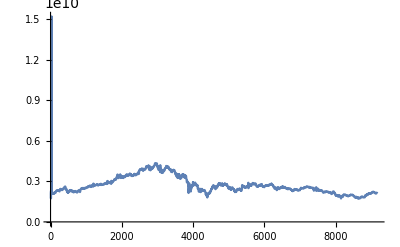

```mathematica
ListLinePlot[twapsWethUsdc90d, PlotRange->All]
```

```mathematica
(* Same issues here for early data as UNI/WETH. Cut off first 40 elements *)
twapsWethUsdc90dFiltered = Table[twapsWethUsdc90d[[i]], {i, 40, Length[twapsWethUsdc90d]}]
```

{2.20799×10^9,2.20533×10^9,2.20572×10^9,2.20558×10^9,2.20476×10^9,2.2039×10^9,2.20513×10^9,2.2031×10^9,2.1997×10^9,2.1977×10^9,2.19642×10^9,2.19264×10^9,2.18452×10^9,2.17974×10^9,2.17409×10^9,2.16595×10^9,2.15763×10^9,2.14687×10^9,2.13229×10^9,2.11795×10^9,2.10658×10^9,2.10155×10^9,2.10459×10^9,2.10836×10^9,2.11006×10^9,2.10998×10^9,2.10671×10^9,2.09959×10^9,2.09156×10^9,2.08485×10^9,2.07922×10^9,2.07646×10^9,2.07685×10^9,2.08201×10^9,2.08605×10^9,2.0936×10^9,2.09635×10^9,2.10078×10^9,2.1063×10^9,2.11173×10^9,2.11541×10^9,2.12081×10^9,2.12707×10^9,2.13185×10^9,2.13614×10^9,2.13829×10^9,2.1356×10^9,2.13202×10^9,2.12948×10^9,2.12444×10^9,2.12109×10^9,2.11405×10^9,2.10656×10^9,2.09709×10^9,2.08876×10^9,2.08203×10^9,2.07571×10^9,2.076×10^9,2.07804×10^9,2.0826×10^9,2.092×10^9,2.10137×10^9,2.11342×10^9,2.12133×10^9,2.133×10^9,2.13803×10^9,2.14019×10^9,2.14584×10^9,2.14715×10^9,2.14686×10^9,2.14686×10^9,2.14853×10^9,2.15282×10^9,2.15936×10^9,2.16644×10^9,2.17366×10^9,2.18035×10^9,2.18508×10^9,2.18679×10^9,2.18661×10^9,2.18817×10^9,2.18892×10^9,2.18838×10^9,2.18555×10^9,2.18398×10^9,2.18084×10^9,2.17902×10^9,2.1791×10^9,2.18103×10^9,2.18514×10^9,2.19238×10^9,2.1997×10^9,2.20797×10^9,2.21494×10^9,2.21708×10^9,2.21531×10^9,2.20923×10^9,2.20054×10^9,2.19002×10^9,2.1798×10^9,2.17015×10^9,2.16504×10^9,2.16313×10^9,2.16575×10^9,2.17722×10^9,2.18669×10^9,2.20064×10^9,2.21318×10^9,2.2252×10^9,2.23608×10^9,2.24299×10^9,2.25221×10^9,2.25492×10^9,2.25937×10^9,2.2656×10^9,2.26918×10^9,2.27751×10^9,2.28222×10^9,2.28527×10^9,2.28614×10^9,2.28598×10^9,2.28635×10^9,2.29055×10^9,2.29529×10^9,2.30221×10^9,2.30863×10^9,2.31448×10^9,2.31796×10^9,2.31814×10^9,2.31637×10^9,2.31586×10^9,2.3173×10^9,2.31787×10^9,2.32308×10^9,2.32914×10^9,2.33406×10^9,2.33557×10^9,2.3385×10^9,2.33849×10^9,2.33491×10^9,2.33032×10^9,2.32851×10^9,2.32627×10^9,2.32693×10^9,2.327×10^9,2.32861×10^9,2.32872×10^9,2.3323×10^9,2.33609×10^9,2.34017×10^9,2.34079×10^9,2.33792×10^9,2.32664×10^9,2.31713×10^9,2.30791×10^9,2.30481×10^9,2.30593×10^9,2.31122×10^9,2.31633×10^9,2.31671×10^9,2.31654×10^9,2.31869×10^9,2.31917×10^9,2.32151×10^9,2.32353×10^9,2.32558×10^9,2.32512×10^9,2.32216×10^9,2.31566×10^9,2.30797×10^9,2.30158×10^9,2.30019×10^9,2.29582×10^9,2.29745×10^9,2.29969×10^9,2.3025×10^9,2.30329×10^9,2.30422×10^9,2.30287×10^9,2.3013×10^9,2.30039×10^9,2.30185×10^9,2.30393×10^9,2.30631×10^9,2.31256×10^9,2.31628×10^9,2.31432×10^9,2.31156×10^9,2.30752×10^9,2.30176×10^9,2.29729×10^9,2.29414×10^9,2.2911×10^9,2.28937×10^9,2.28748×10^9,2.28608×10^9,2.2887×10^9,2.29112×10^9,2.29267×10^9,2.29639×10^9,2.29873×10^9,2.30062×10^9,2.30202×10^9,2.3014×10^9,2.29931×10^9,2.29393×10^9,2.28801×10^9,2.28086×10^9,2.27559×10^9,2.27101×10^9,2.26585×10^9,2.26218×10^9,2.25884×10^9,2.25879×10^9,2.26032×10^9,2.27399×10^9,2.28924×10^9,2.31057×10^9,2.32906×10^9,2.35018×10^9,2.35935×10^9,2.36454×10^9,2.36951×10^9,2.37057×10^9,2.37302×10^9,2.37608×10^9,2.37666×10^9,2.37942×10^9,2.38804×10^9,2.3999×10^9,2.41264×10^9,2.42281×10^9,2.43272×10^9,2.43379×10^9,2.43288×10^9,2.43142×10^9,2.43641×10^9,2.44261×10^9,2.44738×10^9,2.44744×10^9,2.44522×10^9,2.43939×10^9,2.43497×10^9,2.43264×10^9,2.42861×10^9,2.42458×10^9,2.42349×10^9,2.42339×10^9,2.42106×10^9,2.41978×10^9,2.41792×10^9,2.41518×10^9,2.41306×10^9,2.41496×10^9,2.42005×10^9,2.42622×10^9,2.43092×10^9,2.43237×10^9,2.43004×10^9,2.42582×10^9,2.42046×10^9,2.41259×10^9,2.40775×10^9,2.40375×10^9,2.39108×10^9,2.39655×10^9,2.3956×10^9,2.39224×10^9,2.38944×10^9,2.39842×10^9,2.38836×10^9,2.38184×10^9,2.3781×10^9,2.3728×10^9,2.36321×10^9,2.35704×10^9,2.35824×10^9,2.36068×10^9,2.3603×10^9,2.36015×10^9,2.3579×10^9,2.35752×10^9,2.35909×10^9,2.36502×10^9,2.37908×10^9,2.39834×10^9,2.4127×10^9,2.42598×10^9,2.43401×10^9,2.43222×10^9,2.41886×10^9,2.40246×10^9,2.39316×10^9,2.38761×10^9,2.38868×10^9,2.40099×10^9,2.41134×10^9,2.41463×10^9,2.41221×10^9,2.40891×10^9,2.40558×10^9,2.40312×10^9,2.40413×10^9,2.41017×10^9,2.41718×10^9,2.4245×10^9,2.43149×10^9,2.43396×10^9,2.43713×10^9,2.43943×10^9,2.44341×10^9,2.45213×10^9,2.45836×10^9,2.47155×10^9,2.47967×10^9,2.48092×10^9,2.48045×10^9,2.47832×10^9,2.47252×10^9,2.46923×10^9,2.46871×10^9,2.46728×10^9,2.46567×10^9,2.46427×10^9,2.45963×10^9,2.45423×10^9,2.44689×10^9,2.44154×10^9,2.43926×10^9,2.44175×10^9,2.44538×10^9,2.45511×10^9,2.46241×10^9,2.47271×10^9,2.47959×10^9,2.48489×10^9,2.48836×10^9,2.49389×10^9,2.49936×10^9,2.50627×10^9,2.51533×10^9,2.52654×10^9,2.53708×10^9,2.54547×10^9,2.55359×10^9,2.56074×10^9,2.5665×10^9,2.57023×10^9,2.57431×10^9,2.57599×10^9,2.57284×10^9,2.57025×10^9,2.56978×10^9,2.56996×10^9,2.56804×10^9,2.56612×10^9,2.56696×10^9,2.56592×10^9,2.56733×10^9,2.57437×10^9,2.58211×10^9,2.58779×10^9,2.59054×10^9,2.59214×10^9,2.59185×10^9,2.59371×10^9,2.59943×10^9,2.60624×10^9,2.61565×10^9,2.6257×10^9,2.62317×10^9,2.61751×10^9,2.60893×10^9,2.59826×10^9,2.56573×10^9,2.55281×10^9,2.54389×10^9,2.54209×10^9,2.54473×10^9,2.54821×10^9,2.54514×10^9,2.53653×10^9,2.52562×10^9,2.51813×10^9,2.5154×10^9,2.51558×10^9,2.51916×10^9,2.51323×10^9,2.49936×10^9,2.48124×10^9,2.45851×10^9,2.42959×10^9,2.40366×10^9,2.39405×10^9,2.38788×10^9,2.38704×10^9,2.39695×10^9,2.41192×10^9,2.41702×10^9,2.41739×10^9,2.4192×10^9,2.41777×10^9,2.4136×10^9,2.41326×10^9,2.4183×10^9,2.42198×10^9,2.42571×10^9,2.42369×10^9,2.41881×10^9,2.41632×10^9,2.417×10^9,2.41421×10^9,2.41041×10^9,2.40525×10^9,2.39325×10^9,2.3742×10^9,2.35997×10^9,2.34364×10^9,2.33289×10^9,2.31322×10^9,2.28152×10^9,2.25267×10^9,2.2342×10^9,2.21876×10^9,2.21877×10^9,2.20542×10^9,2.24012×10^9,2.25011×10^9,2.25639×10^9,2.26274×10^9,2.28594×10^9,2.25998×10^9,2.25792×10^9,2.24987×10^9,2.23585×10^9,2.23095×10^9,2.21622×10^9,2.20627×10^9,2.20518×10^9,2.20774×10^9,2.20858×10^9,2.21536×10^9,2.21222×10^9,2.201×10^9,2.19372×10^9,2.18937×10^9,2.1898×10^9,2.19679×10^9,2.19911×10^9,2.1922×10^9,2.1814×10^9,2.16775×10^9,2.15329×10^9,2.14905×10^9,2.15453×10^9,2.16311×10^9,2.17754×10^9,2.1886×10^9,2.19496×10^9,2.19521×10^9,2.19642×10^9,2.19586×10^9,2.20198×10^9,2.21422×10^9,2.22915×10^9,2.24864×10^9,2.26186×10^9,2.26818×10^9,2.27401×10^9,2.27947×10^9,2.28488×10^9,2.28763×10^9,2.29374×10^9,2.2935×10^9,2.28949×10^9,2.28122×10^9,2.27718×10^9,2.26861×10^9,2.26267×10^9,2.25558×10^9,2.24668×10^9,2.23444×10^9,2.22963×10^9,2.22708×10^9,2.23103×10^9,2.2414×10^9,2.25694×10^9,2.26796×10^9,2.27638×10^9,2.28157×10^9,2.28064×10^9,2.28194×10^9,2.28855×10^9,2.29747×10^9,2.30827×10^9,2.32178×10^9,2.32668×10^9,2.33208×10^9,2.33238×10^9,2.3302×10^9,2.32706×10^9,2.32483×10^9,2.31294×10^9,2.30725×10^9,2.30586×10^9,2.30549×10^9,2.30875×10^9,2.32069×10^9,2.3289×10^9,2.33887×10^9,2.34455×10^9,2.34705×10^9,2.34831×10^9,2.34906×10^9,2.35316×10^9,2.35714×10^9,2.35986×10^9,2.36222×10^9,2.3601×10^9,2.3539×10^9,2.34852×10^9,2.34723×10^9,2.34445×10^9,2.34153×10^9,2.33929×10^9,2.33339×10^9,2.32678×10^9,2.32081×10^9,2.31699×10^9,2.31726×10^9,2.32052×10^9,2.32377×10^9,2.32889×10^9,2.33394×10^9,2.33811×10^9,2.34591×10^9,2.35097×10^9,2.3484×10^9,2.35168×10^9,2.32961×10^9,2.31129×10^9,2.29316×10^9,2.28242×10^9,2.26549×10^9,2.27423×10^9,2.27616×10^9,2.27699×10^9,2.27214×10^9,2.26531×10^9,2.26117×10^9,2.26262×10^9,2.26374×10^9,2.27259×10^9,2.28756×10^9,2.29605×10^9,2.30558×10^9,2.31085×10^9,2.31211×10^9,2.30824×10^9,2.30791×10^9,2.30698×10^9,2.30738×10^9,2.30927×10^9,2.31281×10^9,2.31167×10^9,2.31119×10^9,2.31043×10^9,2.31036×10^9,2.31235×10^9,2.31484×10^9,2.31729×10^9,2.31702×10^9,2.31256×10^9,2.30616×10^9,2.30047×10^9,2.29057×10^9,2.28115×10^9,2.27844×10^9,2.27622×10^9,2.27517×10^9,2.27651×10^9,2.28024×10^9,2.2841×10^9,2.28743×10^9,2.29157×10^9,2.29036×10^9,2.28662×10^9,2.2796×10^9,2.27321×10^9,2.26679×10^9,2.26409×10^9,2.25823×10^9,2.25215×10^9,2.24222×10^9,2.2328×10^9,2.22194×10^9,2.21341×10^9,2.20809×10^9,2.20552×10^9,2.20414×10^9,2.19895×10^9,2.19647×10^9,2.19691×10^9,2.19647×10^9,2.19503×10^9,2.20427×10^9,2.21535×10^9,2.2193×10^9,2.22389×10^9,2.22751×10^9,2.22651×10^9,2.22377×10^9,2.22182×10^9,2.21675×10^9,2.21353×10^9,2.2085×10^9,2.2066×10^9,2.2045×10^9,2.20086×10^9,2.20024×10^9,2.20296×10^9,2.2091×10^9,2.21676×10^9,2.23307×10^9,2.24249×10^9,2.24753×10^9,2.25021×10^9,2.24966×10^9,2.24755×10^9,2.2456×10^9,2.23852×10^9,2.23414×10^9,2.2323×10^9,2.23331×10^9,2.23724×10^9,2.25193×10^9,2.26192×10^9,2.2681×10^9,2.27309×10^9,2.27821×10^9,2.27709×10^9,2.27605×10^9,2.2762×10^9,2.27657×10^9,2.2759×10^9,2.27331×10^9,2.27229×10^9,2.27357×10^9,2.27615×10^9,2.27991×10^9,2.28524×10^9,2.28907×10^9,2.28996×10^9,2.28935×10^9,2.28902×10^9,2.28737×10^9,2.28427×10^9,2.28126×10^9,2.27787×10^9,2.2695×10^9,2.2637×10^9,2.25955×10^9,2.25705×10^9,2.25289×10^9,2.24485×10^9,2.23883×10^9,2.23579×10^9,2.23314×10^9,2.22735×10^9,2.22636×10^9,2.22483×10^9,2.22245×10^9,2.2202×10^9,2.22366×10^9,2.22793×10^9,2.23311×10^9,2.23822×10^9,2.24126×10^9,2.2419×10^9,2.2428×10^9,2.2431×10^9,2.24391×10^9,2.24438×10^9,2.24251×10^9,2.23764×10^9,2.23285×10^9,2.22346×10^9,2.21278×10^9,2.20363×10^9,2.19764×10^9,2.19271×10^9,2.18978×10^9,2.18801×10^9,2.18846×10^9,2.18976×10^9,2.19189×10^9,2.19508×10^9,2.19872×10^9,2.19979×10^9,2.20061×10^9,2.20091×10^9,2.20067×10^9,2.20039×10^9,2.19911×10^9,2.19718×10^9,2.19265×10^9,2.18857×10^9,2.18462×10^9,2.18244×10^9,2.18365×10^9,2.18494×10^9,2.18744×10^9,2.19216×10^9,2.19477×10^9,2.20087×10^9,2.20936×10^9,2.21653×10^9,2.22071×10^9,2.2223×10^9,2.2192×10^9,2.22228×10^9,2.22865×10^9,2.23954×10^9,2.25415×10^9,2.26709×10^9,2.27141×10^9,2.27257×10^9,2.26885×10^9,2.26645×10^9,2.26725×10^9,2.26852×10^9,2.27247×10^9,2.27791×10^9,2.28419×10^9,2.29287×10^9,2.29906×10^9,2.30388×10^9,2.30929×10^9,2.31112×10^9,2.31317×10^9,2.31564×10^9,2.31573×10^9,2.31561×10^9,2.31542×10^9,2.31413×10^9,2.31519×10^9,2.31908×10^9,2.32147×10^9,2.32736×10^9,2.33494×10^9,2.33998×10^9,2.34386×10^9,2.34424×10^9,2.34487×10^9,2.34497×10^9,2.34218×10^9,2.34076×10^9,2.3418×10^9,2.34242×10^9,2.34246×10^9,2.34516×10^9,2.34479×10^9,2.34044×10^9,2.33679×10^9,2.33343×10^9,2.3292×10^9,2.32519×10^9,2.32298×10^9,2.31663×10^9,2.30992×10^9,2.3041×10^9,2.29961×10^9,2.29866×10^9,2.29799×10^9,2.29939×10^9,2.2985×10^9,2.29236×10^9,2.28655×10^9,2.28392×10^9,2.2809×10^9,2.27635×10^9,2.26595×10^9,2.25331×10^9,2.24366×10^9,2.22887×10^9,2.2145×10^9,2.21107×10^9,2.21254×10^9,2.21443×10^9,2.22275×10^9,2.23622×10^9,2.24861×10^9,2.2594×10^9,2.26408×10^9,2.27033×10^9,2.2803×10^9,2.28652×10^9,2.29094×10^9,2.2981×10^9,2.31555×10^9,2.3368×10^9,2.35786×10^9,2.3769×10^9,2.39538×10^9,2.40696×10^9,2.41176×10^9,2.41569×10^9,2.42174×10^9,2.42885×10^9,2.4366×10^9,2.44476×10^9,2.44712×10^9,2.44617×10^9,2.44403×10^9,2.44363×10^9,2.44219×10^9,2.44623×10^9,2.44958×10^9,2.45123×10^9,2.45112×10^9,2.45167×10^9,2.45407×10^9,2.45812×10^9,2.46162×10^9,2.46369×10^9,2.46427×10^9,2.46289×10^9,2.45751×10^9,2.45375×10^9,2.45255×10^9,2.4526×10^9,2.45302×10^9,2.45883×10^9,2.46523×10^9,2.47045×10^9,2.47648×10^9,2.48128×10^9,2.48101×10^9,2.47698×10^9,2.47104×10^9,2.46507×10^9,2.46046×10^9,2.45761×10^9,2.45548×10^9,2.45276×10^9,2.44984×10^9,2.44595×10^9,2.44291×10^9,2.44226×10^9,2.44154×10^9,2.43928×10^9,2.43783×10^9,2.44323×10^9,2.45125×10^9,2.45873×10^9,2.47179×10^9,2.48318×10^9,2.48587×10^9,2.48714×10^9,2.48866×10^9,2.49182×10^9,2.49573×10^9,2.50131×10^9,2.50888×10^9,2.51503×10^9,2.51715×10^9,2.51551×10^9,2.5143×10^9,2.51203×10^9,2.50693×10^9,2.50391×10^9,2.49954×10^9,2.49506×10^9,2.49414×10^9,2.49543×10^9,2.49693×10^9,2.4989×10^9,2.49877×10^9,2.49364×10^9,2.49147×10^9,2.48988×10^9,2.48811×10^9,2.48799×10^9,2.48933×10^9,2.49132×10^9,2.49484×10^9,2.49545×10^9,2.49487×10^9,2.48933×10^9,2.48526×10^9,2.48001×10^9,2.48286×10^9,2.49015×10^9,2.50192×10^9,2.50791×10^9,2.51492×10^9,2.51568×10^9,2.51417×10^9,2.50893×10^9,2.50468×10^9,2.50156×10^9,2.49831×10^9,2.49638×10^9,2.49477×10^9,2.49335×10^9,2.49183×10^9,2.49079×10^9,2.48908×10^9,2.48649×10^9,2.48389×10^9,2.48105×10^9,2.47142×10^9,2.46433×10^9,2.45583×10^9,2.45223×10^9,2.45422×10^9,2.46197×10^9,2.47306×10^9,2.4924×10^9,2.50467×10^9,2.51184×10^9,2.51584×10^9,2.51972×10^9,2.51729×10^9,2.51696×10^9,2.51681×10^9,2.51826×10^9,2.52155×10^9,2.52454×10^9,2.52341×10^9,2.52264×10^9,2.52008×10^9,2.51702×10^9,2.51238×10^9,2.51208×10^9,2.51191×10^9,2.51242×10^9,2.51245×10^9,2.5126×10^9,2.51481×10^9,2.51713×10^9,2.51884×10^9,2.52143×10^9,2.5239×10^9,2.52503×10^9,2.52365×10^9,2.51914×10^9,2.51419×10^9,2.50823×10^9,2.50277×10^9,2.49839×10^9,2.49751×10^9,2.49796×10^9,2.49829×10^9,2.49901×10^9,2.50106×10^9,2.50468×10^9,2.50984×10^9,2.51568×10^9,2.52184×10^9,2.52488×10^9,2.52826×10^9,2.53554×10^9,2.53955×10^9,2.54475×10^9,2.54931×10^9,2.55421×10^9,2.55606×10^9,2.55704×10^9,2.558×10^9,2.55742×10^9,2.55613×10^9,2.55383×10^9,2.55188×10^9,2.55033×10^9,2.55004×10^9,2.54953×10^9,2.54977×10^9,2.54832×10^9,2.54754×10^9,2.547×10^9,2.54779×10^9,2.54815×10^9,2.5505×10^9,2.55165×10^9,2.55143×10^9,2.55092×10^9,2.55027×10^9,2.54893×10^9,2.54858×10^9,2.55059×10^9,2.553×10^9,2.55592×10^9,2.55994×10^9,2.56424×10^9,2.56771×10^9,2.57182×10^9,2.57375×10^9,2.57396×10^9,2.57164×10^9,2.56896×10^9,2.56596×10^9,2.5636×10^9,2.56107×10^9,2.55891×10^9,2.5563×10^9,2.55368×10^9,2.55618×10^9,2.56814×10^9,2.57934×10^9,2.59744×10^9,2.61451×10^9,2.62719×10^9,2.63082×10^9,2.6356×10^9,2.64104×10^9,2.64795×10^9,2.65163×10^9,2.65855×10^9,2.65906×10^9,2.65748×10^9,2.65239×10^9,2.65007×10^9,2.64537×10^9,2.6422×10^9,2.63909×10^9,2.63922×10^9,2.63904×10^9,2.63858×10^9,2.63735×10^9,2.63764×10^9,2.63803×10^9,2.63722×10^9,2.63794×10^9,2.6394×10^9,2.63626×10^9,2.6309×10^9,2.62599×10^9,2.62427×10^9,2.62282×10^9,2.62459×10^9,2.62923×10^9,2.63363×10^9,2.63453×10^9,2.63619×10^9,2.63742×10^9,2.6365×10^9,2.63813×10^9,2.63956×10^9,2.63923×10^9,2.63813×10^9,2.63675×10^9,2.63277×10^9,2.62774×10^9,2.6252×10^9,2.62523×10^9,2.62802×10^9,2.63213×10^9,2.63998×10^9,2.65069×10^9,2.66276×10^9,2.67138×10^9,2.67884×10^9,2.6839×10^9,2.68591×10^9,2.68649×10^9,2.68838×10^9,2.69162×10^9,2.69579×10^9,2.69895×10^9,2.70219×10^9,2.70203×10^9,2.6985×10^9,2.69107×10^9,2.68116×10^9,2.6707×10^9,2.65959×10^9,2.65079×10^9,2.6437×10^9,2.64043×10^9,2.63928×10^9,2.63988×10^9,2.6411×10^9,2.64281×10^9,2.6419×10^9,2.63996×10^9,2.63913×10^9,2.63692×10^9,2.63059×10^9,2.629×10^9,2.62375×10^9,2.6125×10^9,2.6043×10^9,2.59472×10^9,2.59248×10^9,2.58477×10^9,2.58679×10^9,2.59057×10^9,2.5975×10^9,2.60157×10^9,2.60817×10^9,2.61214×10^9,2.61509×10^9,2.61697×10^9,2.61809×10^9,2.61915×10^9,2.61857×10^9,2.61463×10^9,2.60977×10^9,2.60421×10^9,2.6001×10^9,2.60019×10^9,2.60194×10^9,2.60676×10^9,2.61245×10^9,2.61714×10^9,2.62146×10^9,2.62891×10^9,2.63716×10^9,2.64614×10^9,2.65821×10^9,2.67367×10^9,2.68377×10^9,2.69346×10^9,2.70188×10^9,2.70791×10^9,2.71172×10^9,2.71441×10^9,2.71902×10^9,2.71242×10^9,2.70675×10^9,2.70174×10^9,2.69608×10^9,2.69353×10^9,2.69857×10^9,2.7032×10^9,2.70851×10^9,2.71255×10^9,2.71347×10^9,2.71033×10^9,2.70519×10^9,2.69555×10^9,2.68986×10^9,2.68374×10^9,2.68337×10^9,2.68503×10^9,2.68906×10^9,2.69365×10^9,2.70085×10^9,2.7055×10^9,2.71066×10^9,2.71477×10^9,2.71774×10^9,2.71978×10^9,2.71976×10^9,2.71957×10^9,2.72293×10^9,2.72605×10^9,2.72826×10^9,2.61748×10^9,2.72971×10^9,2.72785×10^9,2.72473×10^9,2.72449×10^9,2.83875×10^9,2.73048×10^9,2.70685×10^9,2.72574×10^9,2.72363×10^9,2.71831×10^9,2.71326×10^9,2.73625×10^9,2.71169×10^9,2.71164×10^9,2.71516×10^9,2.72376×10^9,2.73414×10^9,2.74182×10^9,2.74377×10^9,2.74286×10^9,2.73679×10^9,2.72737×10^9,2.72313×10^9,2.72223×10^9,2.72211×10^9,2.72412×10^9,2.73119×10^9,2.73578×10^9,2.73961×10^9,2.74275×10^9,2.74377×10^9,2.74148×10^9,2.73802×10^9,2.73215×10^9,2.72686×10^9,2.72274×10^9,2.71851×10^9,2.71589×10^9,2.71682×10^9,2.71852×10^9,2.71973×10^9,2.72099×10^9,2.72118×10^9,2.72036×10^9,2.71803×10^9,2.71711×10^9,2.71625×10^9,2.71402×10^9,2.7077×10^9,2.70253×10^9,2.69641×10^9,2.69104×10^9,2.68881×10^9,2.6873×10^9,2.68706×10^9,2.68928×10^9,2.69198×10^9,2.69406×10^9,2.69883×10^9,2.70389×10^9,2.70778×10^9,2.71183×10^9,2.71527×10^9,2.72096×10^9,2.72397×10^9,2.72755×10^9,2.72925×10^9,2.72992×10^9,2.73064×10^9,2.73154×10^9,2.73126×10^9,2.73096×10^9,2.7294×10^9,2.72633×10^9,2.724×10^9,2.72102×10^9,2.71824×10^9,2.72097×10^9,2.72841×10^9,2.73666×10^9,2.74697×10^9,2.75731×10^9,2.7641×10^9,2.76504×10^9,2.76546×10^9,2.76513×10^9,2.76459×10^9,2.76491×10^9,2.76668×10^9,2.76743×10^9,2.76769×10^9,2.76806×10^9,2.76717×10^9,2.76543×10^9,2.76721×10^9,2.77086×10^9,2.775×10^9,2.78064×10^9,2.78663×10^9,2.78752×10^9,2.78625×10^9,2.78341×10^9,2.77901×10^9,2.77219×10^9,2.76783×10^9,2.76488×10^9,2.76346×10^9,2.7638×10^9,2.76513×10^9,2.7666×10^9,2.76932×10^9,2.77417×10^9,2.77752×10^9,2.78108×10^9,2.7845×10^9,2.78344×10^9,2.77817×10^9,2.77243×10^9,2.76555×10^9,2.75762×10^9,2.74739×10^9,2.74127×10^9,2.738×10^9,2.7346×10^9,2.73519×10^9,2.73259×10^9,2.72757×10^9,2.72235×10^9,2.7184×10^9,2.71327×10^9,2.71615×10^9,2.71967×10^9,2.72248×10^9,2.72501×10^9,2.72742×10^9,2.72738×10^9,2.72296×10^9,2.71582×10^9,2.71306×10^9,2.71057×10^9,2.70641×10^9,2.70649×10^9,2.70927×10^9,2.7094×10^9,2.70879×10^9,2.71196×10^9,2.71795×10^9,2.72507×10^9,2.73315×10^9,2.74055×10^9,2.74832×10^9,2.7532×10^9,2.75747×10^9,2.76008×10^9,2.76143×10^9,2.76196×10^9,2.76191×10^9,2.76149×10^9,2.75977×10^9,2.7548×10^9,2.75368×10^9,2.75089×10^9,2.7477×10^9,2.74435×10^9,2.74318×10^9,2.73905×10^9,2.73823×10^9,2.73931×10^9,2.74195×10^9,2.74371×10^9,2.74567×10^9,2.74399×10^9,2.74219×10^9,2.7421×10^9,2.74112×10^9,2.74029×10^9,2.74087×10^9,2.74219×10^9,2.74109×10^9,2.7422×10^9,2.74414×10^9,2.74721×10^9,2.75003×10^9,2.75336×10^9,2.75674×10^9,2.75873×10^9,2.76045×10^9,2.76198×10^9,2.7632×10^9,2.76403×10^9,2.76461×10^9,2.76565×10^9,2.76728×10^9,2.77046×10^9,2.77379×10^9,2.77742×10^9,2.78123×10^9,2.78293×10^9,2.7827×10^9,2.78245×10^9,2.78097×10^9,2.77977×10^9,2.77746×10^9,2.77616×10^9,2.77466×10^9,2.77401×10^9,2.77533×10^9,2.7787×10^9,2.78216×10^9,2.80134×10^9,2.78906×10^9,2.78842×10^9,2.78723×10^9,2.82806×10^9,2.76798×10^9,2.78159×10^9,2.7813×10^9,2.77825×10^9,2.72922×10^9,2.76753×10^9,2.76317×10^9,2.75753×10^9,2.75353×10^9,2.75102×10^9,2.7483×10^9,2.74567×10^9,2.74392×10^9,2.74468×10^9,2.74638×10^9,2.74819×10^9,2.7477×10^9,2.74719×10^9,2.74595×10^9,2.74403×10^9,2.74128×10^9,2.74355×10^9,2.74612×10^9,2.7494×10^9,2.75331×10^9,2.75533×10^9,2.75248×10^9,2.7507×10^9,2.74822×10^9,2.74593×10^9,2.7459×10^9,2.74559×10^9,2.74579×10^9,2.74671×10^9,2.74729×10^9,2.7484×10^9,2.75239×10^9,2.75614×10^9,2.75919×10^9,2.76152×10^9,2.7637×10^9,2.76366×10^9,2.76471×10^9,2.76466×10^9,2.76468×10^9,2.76518×10^9,2.76498×10^9,2.76413×10^9,2.76529×10^9,2.76855×10^9,2.77194×10^9,2.77473×10^9,2.77689×10^9,2.77822×10^9,2.77799×10^9,2.77618×10^9,2.77409×10^9,2.77224×10^9,2.76982×10^9,2.76719×10^9,2.7649×10^9,2.7613×10^9,2.75929×10^9,2.75776×10^9,2.75645×10^9,2.75597×10^9,2.75652×10^9,2.75541×10^9,2.7544×10^9,2.75292×10^9,2.75267×10^9,2.75227×10^9,2.7536×10^9,2.75607×10^9,2.75943×10^9,2.76309×10^9,2.76715×10^9,2.76933×10^9,2.77048×10^9,2.77078×10^9,2.77071×10^9,2.76979×10^9,2.76909×10^9,2.76776×10^9,2.76768×10^9,2.76883×10^9,2.77949×10^9,2.79242×10^9,2.80527×10^9,2.81563×10^9,2.82967×10^9,2.83186×10^9,2.83186×10^9,2.83116×10^9,2.83322×10^9,2.83502×10^9,2.83731×10^9,2.8405×10^9,2.84328×10^9,2.84375×10^9,2.84361×10^9,2.84323×10^9,2.84274×10^9,2.84259×10^9,2.84563×10^9,2.85031×10^9,2.85527×10^9,2.85864×10^9,2.86233×10^9,2.86076×10^9,2.85856×10^9,2.85557×10^9,2.85439×10^9,2.85513×10^9,2.85625×10^9,2.85655×10^9,2.85682×10^9,2.85649×10^9,2.85557×10^9,2.85521×10^9,2.85615×10^9,2.85757×10^9,2.85818×10^9,2.8577×10^9,2.85372×10^9,2.84594×10^9,2.83934×10^9,2.83444×10^9,2.8325×10^9,2.83316×10^9,2.83598×10^9,2.8374×10^9,2.83687×10^9,2.83468×10^9,2.83461×10^9,2.83743×10^9,2.84098×10^9,2.84543×10^9,2.84947×10^9,2.8527×10^9,2.854×10^9,2.8552×10^9,2.85894×10^9,2.8634×10^9,2.86716×10^9,2.87105×10^9,2.87345×10^9,2.87385×10^9,2.87273×10^9,2.87143×10^9,2.86996×10^9,2.86907×10^9,2.86878×10^9,2.86857×10^9,2.86782×10^9,2.86742×10^9,2.86603×10^9,2.8637×10^9,2.86046×10^9,2.85818×10^9,2.85434×10^9,2.8527×10^9,2.85328×10^9,2.85804×10^9,2.86276×10^9,2.86969×10^9,2.87547×10^9,2.80645×10^9,2.88817×10^9,2.89516×10^9,2.90277×10^9,2.90995×10^9,2.99492×10^9,2.92215×10^9,2.92512×10^9,2.9281×10^9,2.93023×10^9,2.93112×10^9,2.9317×10^9,2.93274×10^9,2.93337×10^9,2.93337×10^9,2.93266×10^9,2.92963×10^9,2.92575×10^9,2.92503×10^9,2.92361×10^9,2.9247×10^9,2.9292×10^9,2.93421×10^9,2.93769×10^9,3.03478×10^9,2.93804×10^9,2.93441×10^9,2.93127×10^9,2.92849×10^9,2.84973×10^9,2.9289×10^9,2.93166×10^9,2.93378×10^9,2.93654×10^9,2.93757×10^9,2.93919×10^9,2.94188×10^9,2.94373×10^9,2.94649×10^9,2.94615×10^9,2.94533×10^9,2.94334×10^9,2.9416×10^9,2.93936×10^9,2.93819×10^9,2.93651×10^9,2.93576×10^9,2.93568×10^9,2.93596×10^9,2.93709×10^9,2.93933×10^9,2.94297×10^9,2.94542×10^9,2.94764×10^9,2.94994×10^9,2.95137×10^9,2.9515×10^9,2.95024×10^9,2.94409×10^9,2.93685×10^9,2.92533×10^9,2.91281×10^9,2.91113×10^9,2.91184×10^9,2.91191×10^9,2.91431×10^9,2.91738×10^9,2.91731×10^9,2.91522×10^9,2.91575×10^9,2.91633×10^9,2.9172×10^9,2.91769×10^9,2.91803×10^9,2.91747×10^9,2.91558×10^9,2.90994×10^9,2.90433×10^9,2.89991×10^9,2.89507×10^9,2.89195×10^9,2.88844×10^9,2.88498×10^9,2.87998×10^9,2.87532×10^9,2.87316×10^9,2.87376×10^9,2.875×10^9,2.87711×10^9,2.87898×10^9,2.88206×10^9,2.88564×10^9,2.89221×10^9,2.89905×10^9,2.90687×10^9,2.91168×10^9,2.9154×10^9,2.91581×10^9,2.91519×10^9,2.91474×10^9,2.91469×10^9,2.91541×10^9,2.91761×10^9,2.9211×10^9,2.92439×10^9,2.92719×10^9,2.92829×10^9,2.92738×10^9,2.92673×10^9,2.92583×10^9,2.92599×10^9,2.92453×10^9,2.92212×10^9,2.92077×10^9,2.91849×10^9,2.9166×10^9,2.9168×10^9,2.91798×10^9,2.91889×10^9,2.91928×10^9,2.91902×10^9,2.81586×10^9,2.91997×10^9,2.92207×10^9,2.92466×10^9,2.92757×10^9,3.04472×10^9,2.93313×10^9,2.93374×10^9,2.93474×10^9,2.93518×10^9,2.93494×10^9,2.93477×10^9,2.93473×10^9,2.93493×10^9,2.93632×10^9,2.938×10^9,2.94001×10^9,2.94144×10^9,2.94487×10^9,2.94892×10^9,2.95266×10^9,2.9592×10^9,2.96545×10^9,2.96951×10^9,2.97281×10^9,2.97447×10^9,2.97448×10^9,2.97352×10^9,2.97196×10^9,2.97037×10^9,2.96885×10^9,2.96757×10^9,2.96789×10^9,2.96959×10^9,2.97161×10^9,2.97374×10^9,2.97396×10^9,2.97038×10^9,2.96509×10^9,2.95729×10^9,2.94817×10^9,2.94357×10^9,2.94192×10^9,2.94294×10^9,2.94426×10^9,2.94644×10^9,2.95175×10^9,2.95794×10^9,2.96718×10^9,2.97438×10^9,2.98319×10^9,2.98637×10^9,2.98854×10^9,2.99013×10^9,2.99205×10^9,2.99826×10^9,3.00421×10^9,3.00858×10^9,3.01404×10^9,3.01764×10^9,3.01749×10^9,3.01875×10^9,3.02059×10^9,3.02486×10^9,3.02954×10^9,3.03463×10^9,3.03939×10^9,3.04473×10^9,3.04978×10^9,3.05285×10^9,3.0543×10^9,3.05471×10^9,3.0537×10^9,3.05238×10^9,3.05422×10^9,3.05571×10^9,3.06099×10^9,3.0702×10^9,3.08027×10^9,3.08642×10^9,3.08984×10^9,3.09292×10^9,3.09329×10^9,3.09247×10^9,3.09069×10^9,3.0893×10^9,3.09236×10^9,3.10229×10^9,3.11249×10^9,3.12166×10^9,3.13349×10^9,3.14192×10^9,3.14816×10^9,3.1563×10^9,3.16645×10^9,3.17416×10^9,3.17874×10^9,3.1755×10^9,3.17232×10^9,3.16874×10^9,3.16586×10^9,3.16861×10^9,3.16742×10^9,3.16414×10^9,3.1593×10^9,3.15435×10^9,3.14781×10^9,3.14722×10^9,3.14946×10^9,3.15466×10^9,3.15986×10^9,3.16539×10^9,3.16726×10^9,3.16749×10^9,3.16459×10^9,3.15916×10^9,3.1508×10^9,3.14581×10^9,3.14291×10^9,3.13797×10^9,3.13545×10^9,3.13475×10^9,3.12745×10^9,3.12068×10^9,3.11636×10^9,3.11706×10^9,3.11962×10^9,3.12807×10^9,3.14131×10^9,3.1519×10^9,3.15746×10^9,3.1652×10^9,3.17054×10^9,3.17034×10^9,3.17038×10^9,3.17194×10^9,3.17099×10^9,3.16982×10^9,3.17997×10^9,3.19805×10^9,3.21332×10^9,3.2328×10^9,3.25006×10^9,3.26408×10^9,3.26847×10^9,3.27346×10^9,3.28292×10^9,3.28874×10^9,3.29368×10^9,3.30162×10^9,3.30984×10^9,3.31551×10^9,3.31525×10^9,3.30975×10^9,3.30738×10^9,3.30371×10^9,3.29632×10^9,3.29271×10^9,3.2954×10^9,3.291×10^9,3.28432×10^9,3.28393×10^9,3.28365×10^9,3.28322×10^9,3.28341×10^9,3.28726×10^9,3.28674×10^9,3.29249×10^9,3.30197×10^9,3.32134×10^9,3.34054×10^9,3.35925×10^9,3.37253×10^9,3.38068×10^9,3.38782×10^9,3.39434×10^9,3.40513×10^9,3.41667×10^9,3.42637×10^9,3.51266×10^9,3.41029×10^9,3.39725×10^9,3.38664×10^9,3.35792×10^9,3.24986×10^9,3.32865×10^9,3.31206×10^9,3.29581×10^9,3.29777×10^9,3.30036×10^9,3.29862×10^9,3.28909×10^9,3.27985×10^9,3.27262×10^9,3.25998×10^9,3.24619×10^9,3.24303×10^9,3.24156×10^9,3.24031×10^9,3.24427×10^9,3.24642×10^9,3.24701×10^9,3.25556×10^9,3.26539×10^9,3.27686×10^9,3.29305×10^9,3.31134×10^9,3.32849×10^9,3.34022×10^9,3.35294×10^9,3.35822×10^9,3.36525×10^9,3.3693×10^9,3.37145×10^9,3.37457×10^9,3.37841×10^9,3.37754×10^9,3.37142×10^9,3.36896×10^9,3.36567×10^9,3.3615×10^9,3.35694×10^9,3.35295×10^9,3.34424×10^9,3.33067×10^9,3.32129×10^9,3.31551×10^9,3.30967×10^9,3.30488×10^9,3.31224×10^9,3.31948×10^9,3.33212×10^9,3.34441×10^9,3.35342×10^9,3.35429×10^9,3.35717×10^9,3.36256×10^9,3.36871×10^9,3.38226×10^9,3.39839×10^9,3.40725×10^9,3.41138×10^9,3.41839×10^9,3.42868×10^9,3.43749×10^9,3.44802×10^9,3.45623×10^9,3.45604×10^9,3.45006×10^9,3.45079×10^9,3.44972×10^9,3.45783×10^9,3.46868×10^9,3.51917×10^9,3.49037×10^9,3.48956×10^9,3.49155×10^9,3.48313×10^9,3.4358×10^9,3.43892×10^9,3.42236×10^9,3.39615×10^9,3.37087×10^9,3.34657×10^9,3.31593×10^9,3.29004×10^9,3.28075×10^9,3.27893×10^9,3.2681×10^9,3.25206×10^9,3.25651×10^9,3.26333×10^9,3.266×10^9,3.27289×10^9,3.29005×10^9,3.30333×10^9,3.30959×10^9,3.31795×10^9,3.3263×10^9,3.33685×10^9,3.34964×10^9,3.35788×10^9,3.36501×10^9,3.37315×10^9,3.38492×10^9,3.38066×10^9,3.3892×10^9,3.40191×10^9,3.40186×10^9,3.38829×10^9,3.39475×10^9,3.38859×10^9,3.38107×10^9,3.38142×10^9,3.38023×10^9,3.37093×10^9,3.36058×10^9,3.35022×10^9,3.33532×10^9,3.31576×10^9,3.30652×10^9,3.28881×10^9,3.28516×10^9,3.28866×10^9,3.29359×10^9,3.29752×10^9,3.29343×10^9,3.28286×10^9,3.2772×10^9,3.27467×10^9,3.27531×10^9,3.28842×10^9,3.30126×10^9,3.31071×10^9,3.3224×10^9,3.33405×10^9,3.34239×10^9,3.35175×10^9,3.36104×10^9,3.36×10^9,3.3598×10^9,3.35398×10^9,3.34512×10^9,3.33837×10^9,3.32631×10^9,3.31173×10^9,3.30417×10^9,3.29825×10^9,3.29722×10^9,3.29596×10^9,3.29762×10^9,3.3007×10^9,3.30004×10^9,3.29202×10^9,3.28085×10^9,3.27257×10^9,3.26674×10^9,3.26707×10^9,3.2698×10^9,3.27276×10^9,3.27289×10^9,3.26668×10^9,3.25799×10^9,3.25262×10^9,3.25011×10^9,3.25127×10^9,3.25661×10^9,3.26576×10^9,3.27656×10^9,3.29321×10^9,3.31361×10^9,3.32532×10^9,3.3378×10^9,3.34953×10^9,3.35215×10^9,3.35474×10^9,3.35306×10^9,3.35051×10^9,3.3493×10^9,3.35174×10^9,3.36157×10^9,3.37043×10^9,3.37489×10^9,3.3781×10^9,3.37729×10^9,3.37389×10^9,3.37052×10^9,3.36914×10^9,3.36728×10^9,3.36537×10^9,3.36126×10^9,3.35838×10^9,3.36096×10^9,3.36457×10^9,3.3672×10^9,3.3687×10^9,3.37161×10^9,3.37156×10^9,3.37133×10^9,3.37312×10^9,3.37377×10^9,3.37571×10^9,3.37184×10^9,3.36254×10^9,3.34794×10^9,3.33756×10^9,3.33144×10^9,3.3282×10^9,3.32911×10^9,3.33675×10^9,3.33777×10^9,3.33083×10^9,3.32658×10^9,3.32181×10^9,3.32384×10^9,3.33698×10^9,3.35683×10^9,3.37555×10^9,3.40635×10^9,3.42307×10^9,3.42605×10^9,3.42653×10^9,3.42208×10^9,3.41643×10^9,3.41196×10^9,3.41093×10^9,3.41133×10^9,3.41151×10^9,3.41222×10^9,3.41535×10^9,3.4203×10^9,3.42624×10^9,3.43622×10^9,3.44464×10^9,3.45552×10^9,3.46154×10^9,3.46323×10^9,3.46303×10^9,3.46052×10^9,3.45735×10^9,3.45413×10^9,3.45352×10^9,3.45198×10^9,3.4458×10^9,3.44212×10^9,3.43952×10^9,3.44475×10^9,3.4542×10^9,3.47486×10^9,3.48566×10^9,3.50763×10^9,3.5143×10^9,3.5187×10^9,3.52307×10^9,3.52401×10^9,3.52443×10^9,3.52302×10^9,3.51368×10^9,3.50429×10^9,3.49398×10^9,3.48502×10^9,3.47471×10^9,3.47133×10^9,3.46861×10^9,3.47011×10^9,3.47167×10^9,3.47457×10^9,3.47948×10^9,3.48454×10^9,3.48789×10^9,3.48886×10^9,3.4901×10^9,3.48767×10^9,3.48328×10^9,3.47816×10^9,3.47322×10^9,3.46939×10^9,3.47022×10^9,3.47472×10^9,3.47892×10^9,3.48229×10^9,3.48288×10^9,3.47733×10^9,3.46901×10^9,3.45886×10^9,3.45214×10^9,3.45047×10^9,3.4511×10^9,3.45088×10^9,3.45123×10^9,3.44522×10^9,3.43796×10^9,3.42941×10^9,3.42031×10^9,3.41839×10^9,3.41277×10^9,3.41588×10^9,3.42038×10^9,3.42859×10^9,3.43534×10^9,3.43857×10^9,3.44491×10^9,3.44685×10^9,3.44589×10^9,3.44467×10^9,3.44487×10^9,3.44461×10^9,3.44562×10^9,3.44888×10^9,3.4538×10^9,3.46161×10^9,3.46931×10^9,3.47585×10^9,3.48429×10^9,3.48798×10^9,3.48863×10^9,3.48842×10^9,3.49183×10^9,3.49581×10^9,3.50211×10^9,3.50543×10^9,3.50945×10^9,3.50871×10^9,3.50535×10^9,3.49845×10^9,3.49544×10^9,3.49064×10^9,3.48719×10^9,3.48625×10^9,3.48553×10^9,3.48357×10^9,3.48326×10^9,3.48508×10^9,3.48769×10^9,3.49314×10^9,3.50298×10^9,3.51713×10^9,3.53195×10^9,3.54276×10^9,3.552×10^9,3.56154×10^9,3.56924×10^9,3.57419×10^9,3.57553×10^9,3.57612×10^9,3.5747×10^9,3.57416×10^9,3.57271×10^9,3.57542×10^9,3.57985×10^9,3.57558×10^9,3.56714×10^9,3.55475×10^9,3.52847×10^9,3.506×10^9,3.48667×10^9,3.46469×10^9,3.44775×10^9,3.44929×10^9,3.45703×10^9,3.45856×10^9,3.46189×10^9,3.46556×10^9,3.46594×10^9,3.45981×10^9,3.46164×10^9,3.46529×10^9,3.47151×10^9,3.47804×10^9,3.48588×10^9,3.49797×10^9,3.50547×10^9,3.51189×10^9,3.51617×10^9,3.52243×10^9,3.52508×10^9,3.52548×10^9,3.52188×10^9,3.51816×10^9,3.51098×10^9,3.5064×10^9,3.49862×10^9,3.50178×10^9,3.50415×10^9,3.50526×10^9,3.50894×10^9,3.5134×10^9,3.5073×10^9,3.50054×10^9,3.49562×10^9,3.48685×10^9,3.47766×10^9,3.47324×10^9,3.47043×10^9,3.46536×10^9,3.45702×10^9,3.4508×10^9,3.44617×10^9,3.44086×10^9,3.43222×10^9,3.43008×10^9,3.42999×10^9,3.43042×10^9,3.42504×10^9,3.41593×10^9,3.41047×10^9,3.40174×10^9,3.39355×10^9,3.39232×10^9,3.39781×10^9,3.40048×10^9,3.40425×10^9,3.40721×10^9,3.41089×10^9,3.41145×10^9,3.41513×10^9,3.42119×10^9,3.42648×10^9,3.43154×10^9,3.43707×10^9,3.44033×10^9,3.44466×10^9,3.44982×10^9,3.45443×10^9,3.45705×10^9,3.45833×10^9,3.45358×10^9,3.44406×10^9,3.43438×10^9,3.42884×10^9,3.42397×10^9,3.42558×10^9,3.43182×10^9,3.43596×10^9,3.43922×10^9,3.44556×10^9,3.44838×10^9,3.45155×10^9,3.45631×10^9,3.46055×10^9,3.46326×10^9,3.46416×10^9,3.46344×10^9,3.4616×10^9,3.45656×10^9,3.45483×10^9,3.45399×10^9,3.45334×10^9,3.4524×10^9,3.48259×10^9,3.45006×10^9,3.45084×10^9,3.45551×10^9,3.46291×10^9,3.44362×10^9,3.48645×10^9,3.49336×10^9,3.49991×10^9,3.50422×10^9,3.5041×10^9,3.50287×10^9,3.50247×10^9,3.49927×10^9,3.49578×10^9,3.49292×10^9,3.49464×10^9,3.49896×10^9,3.50403×10^9,3.50865×10^9,3.52156×10^9,3.53279×10^9,3.54307×10^9,3.55467×10^9,3.56184×10^9,3.56177×10^9,3.55953×10^9,3.55826×10^9,3.5549×10^9,3.55463×10^9,3.5554×10^9,3.55588×10^9,3.55096×10^9,3.54634×10^9,3.54119×10^9,3.53287×10^9,3.52885×10^9,3.52548×10^9,3.52295×10^9,3.52355×10^9,3.52329×10^9,3.52053×10^9,3.52009×10^9,3.51894×10^9,3.5189×10^9,3.51917×10^9,3.51978×10^9,3.51727×10^9,3.513×10^9,3.50502×10^9,3.49649×10^9,3.48896×10^9,3.48574×10^9,3.48453×10^9,3.48352×10^9,3.48605×10^9,3.4836×10^9,3.4751×10^9,3.46672×10^9,3.45863×10^9,3.45155×10^9,3.45079×10^9,3.45319×10^9,3.46011×10^9,3.46729×10^9,3.47273×10^9,3.47608×10^9,3.48421×10^9,3.49115×10^9,3.49783×10^9,3.50477×10^9,3.5158×10^9,3.52132×10^9,3.52755×10^9,3.53403×10^9,3.5384×10^9,3.54106×10^9,3.54225×10^9,3.54153×10^9,3.54076×10^9,3.53726×10^9,3.53578×10^9,3.53457×10^9,3.53343×10^9,3.53254×10^9,3.53249×10^9,3.53413×10^9,3.5379×10^9,3.54604×10^9,3.555×10^9,3.56171×10^9,3.56992×10^9,3.57051×10^9,3.5657×10^9,3.56091×10^9,3.55599×10^9,3.55004×10^9,3.54756×10^9,3.546×10^9,3.54357×10^9,3.54105×10^9,3.5373×10^9,3.53342×10^9,3.52933×10^9,3.52608×10^9,3.52486×10^9,3.52497×10^9,3.52657×10^9,3.52903×10^9,3.53244×10^9,3.53782×10^9,3.54737×10^9,3.55503×10^9,3.56132×10^9,3.56555×10^9,3.56615×10^9,3.56188×10^9,3.5572×10^9,3.55476×10^9,3.55486×10^9,3.55928×10^9,3.5612×10^9,3.56232×10^9,3.56165×10^9,3.55885×10^9,3.55148×10^9,3.54795×10^9,3.54436×10^9,3.54423×10^9,3.54521×10^9,3.54639×10^9,3.54656×10^9,3.54602×10^9,3.54691×10^9,3.54778×10^9,3.55148×10^9,3.55441×10^9,3.56148×10^9,3.56937×10^9,3.58262×10^9,3.59933×10^9,3.61527×10^9,3.63149×10^9,3.6437×10^9,3.65117×10^9,3.65586×10^9,3.74326×10^9,3.66334×10^9,3.66661×10^9,3.66961×10^9,3.66529×10^9,3.58062×10^9,3.67276×10^9,3.68607×10^9,3.70349×10^9,3.73005×10^9,3.75874×10^9,3.7727×10^9,3.78864×10^9,3.8036×10^9,3.80744×10^9,3.81306×10^9,3.82212×10^9,3.82237×10^9,3.82177×10^9,3.8259×10^9,3.82697×10^9,3.82686×10^9,3.83094×10^9,3.83128×10^9,3.82934×10^9,3.82333×10^9,3.81804×10^9,3.81513×10^9,3.8205×10^9,3.8228×10^9,3.8334×10^9,3.8387×10^9,3.84762×10^9,3.85025×10^9,3.85652×10^9,3.86521×10^9,3.87248×10^9,3.88772×10^9,3.9009×10^9,3.91286×10^9,3.9101×10^9,3.90859×10^9,3.90165×10^9,3.88923×10^9,3.87884×10^9,3.88083×10^9,3.87914×10^9,3.8787×10^9,3.88338×10^9,3.88987×10^9,3.88709×10^9,3.87769×10^9,3.87059×10^9,3.8657×10^9,3.86086×10^9,3.86243×10^9,3.86859×10^9,3.87537×10^9,3.88022×10^9,3.88178×10^9,3.87943×10^9,3.87686×10^9,3.87545×10^9,3.87447×10^9,3.88122×10^9,3.89524×10^9,3.90199×10^9,3.91966×10^9,3.92358×10^9,3.9207×10^9,3.90401×10^9,3.89336×10^9,3.87701×10^9,3.8737×10^9,3.87154×10^9,3.88374×10^9,3.8963×10^9,3.90608×10^9,3.9156×10^9,3.91413×10^9,3.92121×10^9,3.9208×10^9,3.92473×10^9,3.93227×10^9,3.94533×10^9,3.95065×10^9,3.95786×10^9,3.96287×10^9,3.96081×10^9,3.95864×10^9,3.95562×10^9,3.95397×10^9,3.95018×10^9,3.9494×10^9,3.95063×10^9,3.95068×10^9,3.94702×10^9,3.94391×10^9,3.93913×10^9,3.93279×10^9,3.92526×10^9,3.91603×10^9,3.90935×10^9,3.90407×10^9,3.89265×10^9,3.88928×10^9,3.88986×10^9,3.88966×10^9,3.89156×10^9,3.90097×10^9,3.90861×10^9,3.91014×10^9,3.90766×10^9,3.89569×10^9,3.87776×10^9,3.85599×10^9,3.83389×10^9,3.81877×10^9,3.79687×10^9,3.78543×10^9,3.78158×10^9,3.78076×10^9,3.77862×10^9,3.78814×10^9,3.79799×10^9,3.80714×10^9,3.8117×10^9,3.82145×10^9,3.82276×10^9,3.82603×10^9,3.82963×10^9,3.83344×10^9,3.83762×10^9,3.84004×10^9,3.84046×10^9,3.85241×10^9,3.87475×10^9,3.89274×10^9,3.91039×10^9,3.92044×10^9,3.93896×10^9,3.93446×10^9,3.92695×10^9,3.92455×10^9,3.92062×10^9,3.9149×10^9,3.91396×10^9,3.91726×10^9,3.91603×10^9,3.9148×10^9,3.9137×10^9,3.91081×10^9,3.90568×10^9,3.90178×10^9,3.89364×10^9,3.88842×10^9,3.88053×10^9,3.87582×10^9,3.87271×10^9,3.87447×10^9,3.87734×10^9,3.88696×10^9,3.89727×10^9,3.90291×10^9,3.91011×10^9,3.91503×10^9,3.91713×10^9,3.91573×10^9,3.91292×10^9,3.91268×10^9,3.91105×10^9,3.90838×10^9,3.90527×10^9,3.90068×10^9,3.89814×10^9,3.89481×10^9,3.89418×10^9,3.89928×10^9,3.90413×10^9,3.90845×10^9,3.91364×10^9,3.91295×10^9,3.91273×10^9,3.91261×10^9,3.91085×10^9,3.90923×10^9,3.90935×10^9,3.90863×10^9,3.90809×10^9,3.9114×10^9,3.91824×10^9,3.92922×10^9,3.93884×10^9,3.94696×10^9,3.95091×10^9,3.95728×10^9,3.96449×10^9,3.97542×10^9,3.98863×10^9,4.00553×10^9,4.02269×10^9,4.03878×10^9,4.04689×10^9,4.05106×10^9,4.05204×10^9,4.05688×10^9,4.06387×10^9,4.07824×10^9,4.09434×10^9,4.10581×10^9,4.11046×10^9,4.11433×10^9,4.1096×10^9,4.11164×10^9,4.11802×10^9,4.12089×10^9,4.12371×10^9,4.12413×10^9,4.12402×10^9,4.12086×10^9,4.11994×10^9,4.12081×10^9,4.12175×10^9,4.11911×10^9,4.11287×10^9,4.10647×10^9,4.1053×10^9,4.10294×10^9,4.1093×10^9,4.12199×10^9,4.13228×10^9,4.13055×10^9,4.12923×10^9,4.12322×10^9,4.11544×10^9,4.10711×10^9,4.10555×10^9,4.09933×10^9,4.09214×10^9,4.07891×10^9,4.06908×10^9,4.06019×10^9,4.04088×10^9,4.0377×10^9,4.04324×10^9,4.05166×10^9,4.06354×10^9,4.08282×10^9,4.09337×10^9,4.10737×10^9,4.11946×10^9,4.1261×10^9,4.13067×10^9,4.13378×10^9,4.13685×10^9,4.13495×10^9,4.12867×10^9,4.12469×10^9,4.11769×10^9,4.11084×10^9,4.09416×10^9,4.08423×10^9,4.08005×10^9,4.08194×10^9,4.08887×10^9,4.10197×10^9,4.1178×10^9,4.14411×10^9,4.15898×10^9,4.17201×10^9,4.18035×10^9,4.17842×10^9,4.17438×10^9,4.17571×10^9,4.17385×10^9,4.16758×10^9,4.16599×10^9,4.16096×10^9,4.15324×10^9,4.14485×10^9,4.13754×10^9,4.13623×10^9,4.13513×10^9,4.13348×10^9,4.13164×10^9,4.12502×10^9,4.11164×10^9,4.08348×10^9,4.0371×10^9,3.98437×10^9,3.94978×10^9,3.91265×10^9,3.88432×10^9,3.88932×10^9,3.90739×10^9,3.92498×10^9,3.94076×10^9,3.96802×10^9,3.99134×10^9,4.00082×10^9,4.01357×10^9,4.02153×10^9,3.85186×10^9,4.00533×10^9,3.99305×10^9,3.97904×10^9,3.96902×10^9,4.13465×10^9,3.94583×10^9,3.94787×10^9,3.95986×10^9,3.95799×10^9,3.948×10^9,3.93562×10^9,3.91788×10^9,3.89444×10^9,3.88262×10^9,3.88678×10^9,3.89112×10^9,3.89406×10^9,3.89697×10^9,3.88851×10^9,3.87404×10^9,3.86068×10^9,3.84955×10^9,3.82838×10^9,3.82168×10^9,3.82463×10^9,3.82746×10^9,3.83452×10^9,3.8513×10^9,3.86618×10^9,3.87339×10^9,3.88578×10^9,3.8937×10^9,3.90141×10^9,3.89917×10^9,3.8946×10^9,3.89215×10^9,3.88863×10^9,3.88553×10^9,3.89406×10^9,3.90707×10^9,3.91958×10^9,3.93413×10^9,3.94034×10^9,3.9459×10^9,3.94848×10^9,3.94808×10^9,3.94747×10^9,3.94697×10^9,3.94368×10^9,3.93986×10^9,3.93445×10^9,3.93142×10^9,3.92677×10^9,3.93244×10^9,3.93591×10^9,3.94447×10^9,3.9596×10^9,3.97429×10^9,3.99649×10^9,4.0189×10^9,4.03843×10^9,4.04758×10^9,4.0512×10^9,4.05322×10^9,4.05116×10^9,4.04583×10^9,4.0316×10^9,4.01485×10^9,3.99749×10^9,3.96917×10^9,3.95836×10^9,3.94772×10^9,3.94967×10^9,3.94708×10^9,3.95243×10^9,3.94382×10^9,3.94227×10^9,3.94069×10^9,3.94402×10^9,3.95375×10^9,3.96281×10^9,3.96818×10^9,3.97542×10^9,3.98022×10^9,3.98711×10^9,3.99905×10^9,4.00156×10^9,4.01059×10^9,4.02501×10^9,4.03681×10^9,4.03996×10^9,4.0411×10^9,4.04201×10^9,4.03566×10^9,4.02696×10^9,4.02386×10^9,4.02746×10^9,4.03039×10^9,4.0344×10^9,4.04182×10^9,4.05218×10^9,4.0643×10^9,4.06866×10^9,4.07165×10^9,4.06711×10^9,4.06119×10^9,4.05768×10^9,4.05645×10^9,4.05441×10^9,4.05656×10^9,4.06441×10^9,4.07113×10^9,4.08582×10^9,4.09817×10^9,4.11539×10^9,4.1267×10^9,4.13384×10^9,4.1404×10^9,4.13459×10^9,4.13162×10^9,4.12614×10^9,4.12262×10^9,4.11788×10^9,4.12311×10^9,4.12381×10^9,4.12715×10^9,4.13142×10^9,4.13466×10^9,4.13899×10^9,4.1451×10^9,4.1554×10^9,4.1597×10^9,4.16642×10^9,4.16956×10^9,4.17178×10^9,4.17319×10^9,4.17379×10^9,4.17413×10^9,4.17599×10^9,4.178×10^9,4.18279×10^9,4.19262×10^9,4.21841×10^9,4.22934×10^9,4.24625×10^9,4.25853×10^9,4.2641×10^9,4.26884×10^9,4.28496×10^9,4.29803×10^9,4.30818×10^9,4.32035×10^9,4.32243×10^9,4.31363×10^9,4.30757×10^9,4.30775×10^9,4.30777×10^9,4.31554×10^9,4.32228×10^9,4.3306×10^9,4.33586×10^9,4.33479×10^9,4.33472×10^9,4.33339×10^9,4.32988×10^9,4.31945×10^9,4.31652×10^9,4.31475×10^9,4.31221×10^9,4.30964×10^9,4.30912×10^9,4.30283×10^9,4.29696×10^9,4.29292×10^9,4.29223×10^9,4.29086×10^9,4.29344×10^9,4.2976×10^9,4.29786×10^9,4.30192×10^9,4.2991×10^9,4.29303×10^9,4.28969×10^9,4.28404×10^9,4.27129×10^9,4.26228×10^9,4.25718×10^9,4.25482×10^9,4.25303×10^9,4.25589×10^9,4.26054×10^9,4.26471×10^9,4.26564×10^9,4.27134×10^9,4.27796×10^9,4.28465×10^9,4.29109×10^9,4.29802×10^9,4.29509×10^9,4.28895×10^9,4.28761×10^9,4.28702×10^9,4.28449×10^9,4.29269×10^9,4.31599×10^9,4.32665×10^9,4.33239×10^9,4.32753×10^9,4.29907×10^9,4.27056×10^9,4.25056×10^9,4.23096×10^9,4.20803×10^9,4.17998×10^9,4.1656×10^9,4.14873×10^9,4.13581×10^9,4.13993×10^9,4.14267×10^9,4.14784×10^9,4.15588×10^9,4.15545×10^9,4.14856×10^9,4.13743×10^9,4.11796×10^9,4.09202×10^9,4.07036×10^9,4.04037×10^9,4.01414×10^9,4.00195×10^9,4.00064×10^9,4.00639×10^9,4.01645×10^9,4.04288×10^9,4.05523×10^9,4.06683×10^9,4.07428×10^9,4.08173×10^9,4.08269×10^9,4.08557×10^9,4.09494×10^9,4.10324×10^9,4.10879×10^9,4.11033×10^9,4.11072×10^9,4.09757×10^9,4.0866×10^9,4.09114×10^9,4.101×10^9,4.10673×10^9,4.10948×10^9,4.09899×10^9,4.06445×10^9,3.97699×10^9,3.9062×10^9,3.86404×10^9,3.84488×10^9,3.83713×10^9,3.87749×10^9,3.91116×10^9,3.93195×10^9,3.94073×10^9,3.94516×10^9,3.95084×10^9,3.9649×10^9,3.97689×10^9,3.99148×10^9,4.00052×10^9,4.00722×10^9,4.00834×10^9,3.99984×10^9,3.98238×10^9,3.96865×10^9,3.95305×10^9,3.92907×10^9,3.92149×10^9,3.92724×10^9,3.93341×10^9,3.94099×10^9,3.9467×10^9,3.94129×10^9,3.93463×10^9,3.93509×10^9,3.94109×10^9,3.95475×10^9,3.97365×10^9,3.98573×10^9,3.99733×10^9,4.00034×10^9,4.00154×10^9,4.00017×10^9,4.00303×10^9,4.00519×10^9,4.00478×10^9,4.00375×10^9,3.99974×10^9,3.70516×10^9,3.97774×10^9,3.96542×10^9,3.95163×10^9,3.94021×10^9,4.20291×10^9,3.8932×10^9,3.87303×10^9,3.84551×10^9,3.81867×10^9,3.78708×10^9,3.76584×10^9,3.75988×10^9,3.75193×10^9,3.74188×10^9,3.73482×10^9,3.71064×10^9,3.6852×10^9,3.67637×10^9,3.67809×10^9,3.69009×10^9,3.7175×10^9,3.73143×10^9,3.75276×10^9,3.76666×10^9,3.77533×10^9,3.79091×10^9,3.80972×10^9,3.80562×10^9,3.80911×10^9,3.81998×10^9,3.82782×10^9,3.83836×10^9,3.858×10^9,3.8728×10^9,3.87842×10^9,3.87894×10^9,3.8643×10^9,3.84876×10^9,3.83156×10^9,3.81204×10^9,3.7935×10^9,3.79171×10^9,3.79783×10^9,3.80823×10^9,3.81974×10^9,3.80815×10^9,3.7866×10^9,3.74747×10^9,3.69395×10^9,3.65261×10^9,3.64082×10^9,3.64927×10^9,3.65415×10^9,3.66856×10^9,3.67319×10^9,3.66206×10^9,3.64099×10^9,3.62802×10^9,3.62655×10^9,3.63904×10^9,3.6556×10^9,3.66925×10^9,3.67507×10^9,3.6808×10^9,3.68184×10^9,3.6837×10^9,3.69111×10^9,3.70419×10^9,3.71354×10^9,3.72905×10^9,3.7436×10^9,3.74649×10^9,3.75631×10^9,3.75731×10^9,3.74585×10^9,3.73632×10^9,3.73822×10^9,3.73536×10^9,3.71834×10^9,3.70471×10^9,3.69195×10^9,3.66884×10^9,3.65843×10^9,3.66591×10^9,3.69031×10^9,3.7137×10^9,3.74114×10^9,3.75996×10^9,3.7771×10^9,3.79488×10^9,3.80858×10^9,3.82854×10^9,3.84068×10^9,3.85742×10^9,3.86703×10^9,3.86848×10^9,3.85861×10^9,3.84793×10^9,3.84004×10^9,3.83009×10^9,3.82052×10^9,3.8135×10^9,3.81248×10^9,3.81188×10^9,3.80576×10^9,3.80374×10^9,3.80348×10^9,3.80587×10^9,3.80467×10^9,3.80264×10^9,3.80043×10^9,3.79869×10^9,3.79545×10^9,3.79661×10^9,3.80313×10^9,3.80907×10^9,3.81975×10^9,3.82968×10^9,3.835×10^9,3.84017×10^9,3.83573×10^9,3.82728×10^9,3.82029×10^9,3.82075×10^9,3.82943×10^9,3.84185×10^9,3.85652×10^9,3.86788×10^9,3.87371×10^9,3.87946×10^9,3.88113×10^9,3.88821×10^9,3.8989×10^9,3.90701×10^9,3.91861×10^9,3.93899×10^9,3.95347×10^9,3.95715×10^9,3.96215×10^9,3.96708×10^9,3.96727×10^9,3.96332×10^9,3.96359×10^9,3.96538×10^9,3.9754×10^9,3.98139×10^9,3.99539×10^9,4.00378×10^9,4.01067×10^9,4.01401×10^9,4.01073×10^9,4.00375×10^9,3.99989×10^9,3.99333×10^9,3.98991×10^9,3.98888×10^9,3.9904×10^9,3.991×10^9,3.99628×10^9,4.00986×10^9,4.02117×10^9,4.03532×10^9,4.04613×10^9,4.05591×10^9,4.05978×10^9,4.07181×10^9,4.08964×10^9,4.1101×10^9,4.12565×10^9,4.13557×10^9,4.14346×10^9,4.14819×10^9,4.14689×10^9,4.13953×10^9,4.13699×10^9,4.13251×10^9,4.12609×10^9,4.12334×10^9,4.1271×10^9,4.12435×10^9,4.1194×10^9,4.11599×10^9,4.11084×10^9,4.10086×10^9,4.09684×10^9,4.08958×10^9,4.08225×10^9,4.07492×10^9,4.07146×10^9,4.0673×10^9,4.06102×10^9,4.06048×10^9,4.05844×10^9,4.04483×10^9,4.03704×10^9,4.02716×10^9,4.01433×10^9,4.00694×10^9,4.01143×10^9,4.01332×10^9,4.02135×10^9,4.0288×10^9,4.03247×10^9,4.04564×10^9,4.06069×10^9,4.06911×10^9,4.07811×10^9,4.08954×10^9,4.08947×10^9,4.08735×10^9,4.08853×10^9,4.09105×10^9,4.09529×10^9,4.09122×10^9,4.08772×10^9,4.08315×10^9,4.06805×10^9,4.05367×10^9,4.05716×10^9,4.05915×10^9,4.07135×10^9,4.08834×10^9,4.09795×10^9,4.10043×10^9,4.10002×10^9,4.09633×10^9,4.09197×10^9,4.08866×10^9,4.07991×10^9,4.0731×10^9,4.06326×10^9,4.05349×10^9,4.04811×10^9,4.04452×10^9,4.04299×10^9,4.04247×10^9,4.04254×10^9,4.03915×10^9,4.03361×10^9,4.02976×10^9,4.02445×10^9,4.0155×10^9,4.01218×10^9,4.01559×10^9,4.0196×10^9,4.01826×10^9,4.01783×10^9,4.00578×10^9,3.99349×10^9,3.9788×10^9,3.95909×10^9,3.94742×10^9,3.93752×10^9,3.93218×10^9,3.92996×10^9,3.92946×10^9,3.92676×10^9,3.91848×10^9,3.91376×10^9,3.91814×10^9,3.92165×10^9,3.9173×10^9,3.91287×10^9,3.90952×10^9,3.89983×10^9,3.88475×10^9,3.87476×10^9,3.86729×10^9,3.85392×10^9,3.84696×10^9,3.84537×10^9,3.85319×10^9,3.86077×10^9,3.86792×10^9,3.87548×10^9,3.88051×10^9,3.88384×10^9,3.88701×10^9,3.89636×10^9,3.90272×10^9,3.90553×10^9,3.91314×10^9,3.91834×10^9,3.91385×10^9,3.90982×10^9,3.9062×10^9,3.90051×10^9,3.88868×10^9,3.88203×10^9,3.87844×10^9,3.8802×10^9,3.88163×10^9,3.8911×10^9,3.89863×10^9,3.89764×10^9,3.88925×10^9,3.87519×10^9,3.85675×10^9,3.83288×10^9,3.8112×10^9,3.78852×10^9,3.77324×10^9,3.75417×10^9,3.74964×10^9,3.75195×10^9,3.75167×10^9,3.75406×10^9,3.75859×10^9,3.7601×10^9,3.7561×10^9,3.7538×10^9,3.75383×10^9,3.74847×10^9,3.7327×10^9,3.71723×10^9,3.71138×10^9,3.71137×10^9,3.72038×10^9,3.73879×10^9,3.76266×10^9,3.77701×10^9,3.78842×10^9,3.79554×10^9,3.80199×10^9,3.80225×10^9,3.80331×10^9,3.80418×10^9,3.80375×10^9,3.80488×10^9,3.80815×10^9,3.8016×10^9,3.79629×10^9,3.78581×10^9,3.76917×10^9,3.7466×10^9,3.72712×10^9,3.70084×10^9,3.68271×10^9,3.68499×10^9,3.70206×10^9,3.72393×10^9,3.74674×10^9,3.76983×10^9,3.7813×10^9,3.78777×10^9,3.7941×10^9,3.80971×10^9,3.82092×10^9,3.82389×10^9,3.82489×10^9,3.82798×10^9,3.82806×10^9,3.8274×10^9,3.82716×10^9,3.82573×10^9,3.81908×10^9,3.81205×10^9,3.80678×10^9,3.80746×10^9,3.80786×10^9,3.81309×10^9,3.8177×10^9,3.82191×10^9,3.81736×10^9,3.81479×10^9,3.81177×10^9,3.80858×10^9,3.80405×10^9,3.79932×10^9,3.79695×10^9,3.8055×10^9,3.82047×10^9,3.84291×10^9,3.85581×10^9,3.86446×10^9,3.86402×10^9,3.86225×10^9,3.85114×10^9,3.84846×10^9,3.84334×10^9,3.83576×10^9,3.83204×10^9,3.82653×10^9,3.81438×10^9,3.81169×10^9,3.8067×10^9,3.80405×10^9,3.80544×10^9,3.81012×10^9,3.81295×10^9,3.81772×10^9,3.82244×10^9,3.82612×10^9,3.83045×10^9,3.83302×10^9,3.83784×10^9,3.84138×10^9,3.84076×10^9,3.83861×10^9,3.83397×10^9,3.82396×10^9,3.81755×10^9,3.80794×10^9,3.80186×10^9,3.79059×10^9,3.77531×10^9,3.75618×10^9,3.74056×10^9,3.72866×10^9,3.71073×10^9,3.709×10^9,3.71065×10^9,3.71264×10^9,3.71543×10^9,3.71926×10^9,3.7137×10^9,3.70714×10^9,3.69902×10^9,3.6873×10^9,3.67614×10^9,3.67616×10^9,3.67063×10^9,3.66337×10^9,3.65393×10^9,3.65301×10^9,3.64593×10^9,3.63065×10^9,3.61561×10^9,3.60695×10^9,3.58391×10^9,3.55542×10^9,3.54398×10^9,3.54134×10^9,3.54672×10^9,3.56603×10^9,3.58846×10^9,3.59698×10^9,3.59328×10^9,3.58517×10^9,3.56207×10^9,3.52941×10^9,3.50644×10^9,3.49614×10^9,3.47452×10^9,3.4552×10^9,3.4473×10^9,3.44514×10^9,3.43114×10^9,3.42176×10^9,3.41747×10^9,3.40836×10^9,3.39745×10^9,3.38722×10^9,3.3801×10^9,3.39227×10^9,3.41376×10^9,3.43443×10^9,3.46563×10^9,3.5025×10^9,3.52167×10^9,3.53027×10^9,3.54028×10^9,3.54086×10^9,3.53637×10^9,3.53978×10^9,3.54635×10^9,3.5513×10^9,3.55881×10^9,3.564×10^9,3.55829×10^9,3.55339×10^9,3.54879×10^9,3.53222×10^9,3.51549×10^9,3.48597×10^9,3.46743×10^9,3.43759×10^9,3.42065×10^9,3.41531×10^9,3.41854×10^9,3.42143×10^9,3.41843×10^9,3.41376×10^9,3.40806×10^9,3.3968×10^9,3.38051×10^9,3.3582×10^9,3.3375×10^9,3.3191×10^9,3.2837×10^9,3.25385×10^9,3.2503×10^9,3.25282×10^9,3.25561×10^9,3.27644×10^9,3.29355×10^9,3.29819×10^9,3.29619×10^9,3.29324×10^9,3.28084×10^9,3.294×10^9,3.32167×10^9,3.34413×10^9,3.37912×10^9,3.41236×10^9,3.41805×10^9,3.41972×10^9,3.43337×10^9,3.44422×10^9,3.46301×10^9,3.48328×10^9,3.49395×10^9,3.50439×10^9,3.51771×10^9,3.52385×10^9,3.53029×10^9,3.53401×10^9,3.53384×10^9,3.52425×10^9,3.5185×10^9,3.50984×10^9,3.51009×10^9,3.51055×10^9,3.5079×10^9,3.50481×10^9,3.497×10^9,3.48291×10^9,3.47397×10^9,3.47564×10^9,3.47732×10^9,3.48441×10^9,3.49703×10^9,3.51061×10^9,3.51707×10^9,3.51713×10^9,3.50768×10^9,3.50096×10^9,3.49012×10^9,3.47923×10^9,3.46885×10^9,3.4643×10^9,3.45705×10^9,3.4505×10^9,3.43438×10^9,3.42214×10^9,3.41067×10^9,3.39936×10^9,3.38738×10^9,3.38175×10^9,3.37698×10^9,3.36697×10^9,3.34839×10^9,3.32999×10^9,3.31463×10^9,3.29967×10^9,3.28977×10^9,3.28033×10^9,3.26675×10^9,3.24697×10^9,3.22138×10^9,3.1982×10^9,3.19106×10^9,3.18923×10^9,3.20058×10^9,3.22251×10^9,3.24451×10^9,3.2672×10^9,3.30093×10^9,3.31948×10^9,3.34981×10^9,3.37183×10^9,3.37946×10^9,3.37531×10^9,3.37742×10^9,3.37943×10^9,3.38169×10^9,3.39435×10^9,3.41114×10^9,3.4237×10^9,3.4277×10^9,3.42172×10^9,3.41716×10^9,3.39205×10^9,3.36288×10^9,3.33827×10^9,3.32505×10^9,3.31657×10^9,3.28975×10^9,3.27702×10^9,3.26224×10^9,3.24558×10^9,3.23244×10^9,3.23444×10^9,3.24783×10^9,3.26537×10^9,3.27293×10^9,3.29442×10^9,3.31251×10^9,3.32269×10^9,3.33485×10^9,3.34912×10^9,3.35681×10^9,3.36179×10^9,3.36964×10^9,3.37671×10^9,3.38295×10^9,3.39009×10^9,3.39029×10^9,3.38404×10^9,3.38192×10^9,3.38019×10^9,3.38069×10^9,3.38427×10^9,3.3893×10^9,3.39349×10^9,3.39409×10^9,3.3919×10^9,3.39906×10^9,3.41108×10^9,3.42081×10^9,3.43875×10^9,3.46341×10^9,3.47802×10^9,3.49311×10^9,3.51076×10^9,3.5215×10^9,3.52784×10^9,3.53129×10^9,3.5333×10^9,3.53709×10^9,3.53957×10^9,3.53348×10^9,3.52693×10^9,3.51451×10^9,3.4999×10^9,3.49063×10^9,3.49024×10^9,3.49137×10^9,3.49716×10^9,3.50291×10^9,3.50517×10^9,3.50745×10^9,3.50475×10^9,3.49822×10^9,3.48781×10^9,3.47665×10^9,3.4705×10^9,3.46524×10^9,3.46324×10^9,3.46422×10^9,3.46992×10^9,3.47527×10^9,3.4825×10^9,3.48955×10^9,3.49684×10^9,3.49955×10^9,3.50225×10^9,3.50646×10^9,3.51546×10^9,3.51933×10^9,3.51881×10^9,3.51567×10^9,3.50545×10^9,3.48399×10^9,3.4638×10^9,3.4446×10^9,3.41714×10^9,3.4054×10^9,3.39857×10^9,3.38696×10^9,3.3702×10^9,3.36171×10^9,3.34232×10^9,3.31536×10^9,3.30122×10^9,3.3037×10^9,3.31068×10^9,3.32665×10^9,3.34775×10^9,3.36065×10^9,3.37053×10^9,3.36699×10^9,3.36075×10^9,3.36827×10^9,3.38003×10^9,3.38721×10^9,3.40152×10^9,3.41784×10^9,3.42242×10^9,3.42075×10^9,3.4179×10^9,3.40497×10^9,3.39331×10^9,3.46745×10^9,3.37066×10^9,3.36602×10^9,3.36274×10^9,3.35827×10^9,3.26953×10^9,3.35576×10^9,3.36708×10^9,3.37949×10^9,3.3863×10^9,3.39782×10^9,3.40859×10^9,3.41447×10^9,3.41987×10^9,3.43181×10^9,3.43977×10^9,3.4425×10^9,3.44108×10^9,3.43483×10^9,3.42398×10^9,3.41218×10^9,3.40557×10^9,3.40596×10^9,3.40356×10^9,3.39199×10^9,3.38298×10^9,3.37345×10^9,3.3571×10^9,3.35395×10^9,3.36529×10^9,3.37867×10^9,3.38987×10^9,3.40067×10^9,3.40469×10^9,3.40322×10^9,3.38928×10^9,3.36517×10^9,3.33857×10^9,3.30036×10^9,3.26438×10^9,3.23868×10^9,3.21833×10^9,3.20198×10^9,3.19096×10^9,3.1874×10^9,3.17792×10^9,3.15504×10^9,3.1414×10^9,3.1309×10^9,3.1214×10^9,3.11368×10^9,3.11638×10^9,3.11358×10^9,3.09728×10^9,3.06619×10^9,3.02977×10^9,2.98709×10^9,2.95552×10^9,2.9444×10^9,2.95064×10^9,2.96126×10^9,2.96879×10^9,2.93567×10^9,2.96811×10^9,2.96511×10^9,2.96704×10^9,2.97348×10^9,3.01105×10^9,2.97019×10^9,2.95301×10^9,2.9397×10^9,2.93333×10^9,2.93951×10^9,2.94842×10^9,2.96169×10^9,2.96481×10^9,2.96503×10^9,2.96114×10^9,2.95889×10^9,2.96274×10^9,2.97333×10^9,2.9802×10^9,2.97965×10^9,2.97485×10^9,2.96867×10^9,2.96082×10^9,2.94925×10^9,2.94094×10^9,2.92352×10^9,2.90231×10^9,2.87697×10^9,2.85292×10^9,2.81334×10^9,2.75973×10^9,2.72022×10^9,2.69109×10^9,2.67203×10^9,2.67034×10^9,2.67634×10^9,2.65766×10^9,2.6005×10^9,2.49539×10^9,2.37073×10^9,2.25079×10^9,2.15935×10^9,2.14177×10^9,2.16493×10^9,2.21783×10^9,2.27171×10^9,2.33792×10^9,2.36736×10^9,2.38907×10^9,2.42316×10^9,2.46285×10^9,2.50175×10^9,2.5499×10^9,2.6269×10^9,2.65763×10^9,2.67786×10^9,2.70249×10^9,2.73176×10^9,2.75894×10^9,2.8034×10^9,2.84431×10^9,2.85691×10^9,2.84385×10^9,2.83104×10^9,2.80202×10^9,2.75192×10^9,2.71938×10^9,2.68778×10^9,2.65168×10^9,2.63364×10^9,2.62987×10^9,2.61962×10^9,2.61207×10^9,2.61669×10^9,2.62404×10^9,2.62965×10^9,2.63081×10^9,2.63998×10^9,2.644×10^9,2.60872×10^9,2.57297×10^9,2.54035×10^9,2.52747×10^9,2.52109×10^9,2.52907×10^9,2.54964×10^9,2.58367×10^9,2.61213×10^9,2.63511×10^9,2.65692×10^9,2.66708×10^9,2.65734×10^9,2.64494×10^9,2.62796×10^9,2.59282×10^9,2.55795×10^9,2.53731×10^9,2.51791×10^9,2.48047×10^9,2.43425×10^9,2.37828×10^9,2.32305×10^9,2.27059×10^9,2.25089×10^9,2.2544×10^9,2.27455×10^9,2.29866×10^9,2.33289×10^9,2.35644×10^9,2.37997×10^9,2.40211×10^9,2.42699×10^9,2.44083×10^9,2.45114×10^9,2.45714×10^9,2.45984×10^9,2.47047×10^9,2.45603×10^9,2.50288×10^9,2.51589×10^9,2.53232×10^9,2.5613×10^9,2.61062×10^9,2.57743×10^9,2.5912×10^9,2.6125×10^9,2.62724×10^9,2.62706×10^9,2.62757×10^9,2.63143×10^9,2.63508×10^9,2.63982×10^9,2.65345×10^9,2.67663×10^9,2.70064×10^9,2.71826×10^9,2.72547×10^9,2.73084×10^9,2.72955×10^9,2.71794×10^9,2.70465×10^9,2.69715×10^9,2.68771×10^9,2.67406×10^9,2.65752×10^9,2.64683×10^9,2.64366×10^9,2.64262×10^9,2.65154×10^9,2.66519×10^9,2.67455×10^9,2.67846×10^9,2.68537×10^9,2.68761×10^9,2.69131×10^9,2.69874×10^9,2.71118×10^9,2.71914×10^9,2.73055×10^9,2.75426×10^9,2.78×10^9,2.81168×10^9,2.84145×10^9,2.88063×10^9,2.91068×10^9,2.92932×10^9,2.93362×10^9,2.93724×10^9,2.93834×10^9,2.92258×10^9,2.92069×10^9,2.92673×10^9,2.92367×10^9,2.92148×10^9,2.92897×10^9,2.92825×10^9,2.92525×10^9,2.92122×10^9,2.88556×10^9,2.84109×10^9,2.79943×10^9,2.746×10^9,2.70382×10^9,2.69799×10^9,2.70045×10^9,2.69956×10^9,2.71662×10^9,2.72979×10^9,2.73432×10^9,2.74321×10^9,2.75503×10^9,2.76519×10^9,2.77379×10^9,2.78303×10^9,2.78905×10^9,2.79372×10^9,2.79798×10^9,2.79801×10^9,2.7975×10^9,2.80456×10^9,2.80871×10^9,2.80901×10^9,2.79885×10^9,2.79091×10^9,2.78269×10^9,2.77717×10^9,2.7802×10^9,2.79453×10^9,2.8091×10^9,2.81874×10^9,2.82017×10^9,2.80995×10^9,2.79691×10^9,2.79718×10^9,2.79182×10^9,2.78922×10^9,2.79353×10^9,2.795×10^9,2.78593×10^9,2.78919×10^9,2.79507×10^9,2.80891×10^9,2.83336×10^9,2.85983×10^9,2.87766×10^9,2.89546×10^9,2.90734×10^9,2.91099×10^9,2.90954×10^9,2.90669×10^9,2.89765×10^9,2.88678×10^9,2.87633×10^9,2.86832×10^9,2.85796×10^9,2.85039×10^9,2.8369×10^9,2.82659×10^9,2.81418×10^9,2.80395×10^9,2.79674×10^9,2.81205×10^9,2.78302×10^9,2.77762×10^9,2.77592×10^9,2.77003×10^9,2.74518×10^9,2.7719×10^9,2.77056×10^9,2.76178×10^9,2.75576×10^9,2.7476×10^9,2.74071×10^9,2.7343×10^9,2.73731×10^9,2.74401×10^9,2.74696×10^9,2.74057×10^9,2.7305×10^9,2.71851×10^9,2.70311×10^9,2.68781×10^9,2.6839×10^9,2.68311×10^9,2.68006×10^9,2.68549×10^9,2.70027×10^9,2.70863×10^9,2.7202×10^9,2.73787×10^9,2.74785×10^9,2.75069×10^9,2.75417×10^9,2.75373×10^9,2.75216×10^9,2.74915×10^9,2.73921×10^9,2.72338×10^9,2.7081×10^9,2.69456×10^9,2.68192×10^9,2.68519×10^9,2.6948×10^9,2.7022×10^9,2.70246×10^9,2.69932×10^9,2.68961×10^9,2.67897×10^9,2.67623×10^9,2.6796×10^9,2.68847×10^9,2.70033×10^9,2.71648×10^9,2.70065×10^9,2.66661×10^9,2.61492×10^9,2.57589×10^9,2.53255×10^9,2.51784×10^9,2.51586×10^9,2.51512×10^9,2.50147×10^9,2.47884×10^9,2.45463×10^9,2.44665×10^9,2.45171×10^9,2.45972×10^9,2.46786×10^9,2.47343×10^9,2.47453×10^9,2.46746×10^9,2.46356×10^9,2.46744×10^9,2.47106×10^9,2.4597×10^9,2.44947×10^9,2.4442×10^9,2.44123×10^9,2.43694×10^9,2.44439×10^9,2.44325×10^9,2.42747×10^9,2.40484×10^9,2.38947×10^9,2.35682×10^9,2.33415×10^9,2.32814×10^9,2.32239×10^9,2.30124×10^9,2.28722×10^9,2.25795×10^9,2.24119×10^9,2.23561×10^9,2.25666×10^9,2.27949×10^9,2.31838×10^9,2.34556×10^9,2.36564×10^9,2.37936×10^9,2.38099×10^9,2.38754×10^9,2.39971×10^9,2.40263×10^9,2.40377×10^9,2.40912×10^9,2.41644×10^9,2.41331×10^9,2.41079×10^9,2.40999×10^9,2.41497×10^9,2.41844×10^9,2.42514×10^9,2.43098×10^9,2.44199×10^9,2.4506×10^9,2.45167×10^9,2.45396×10^9,2.46125×10^9,2.46292×10^9,2.45616×10^9,2.44802×10^9,2.43633×10^9,2.42164×10^9,2.39903×10^9,2.38346×10^9,2.36796×10^9,2.35181×10^9,2.33982×10^9,2.33269×10^9,2.31526×10^9,2.3019×10^9,2.28611×10^9,2.2708×10^9,2.25099×10^9,2.23506×10^9,2.22294×10^9,2.22082×10^9,2.21496×10^9,2.21121×10^9,2.21445×10^9,2.21703×10^9,2.21478×10^9,2.21619×10^9,2.21985×10^9,2.21927×10^9,2.22265×10^9,2.22253×10^9,2.2241×10^9,2.23668×10^9,2.25847×10^9,2.2812×10^9,2.30661×10^9,2.33077×10^9,2.34303×10^9,2.34106×10^9,2.33893×10^9,2.34311×10^9,2.34545×10^9,2.34542×10^9,2.3483×10^9,2.35262×10^9,2.35182×10^9,2.36036×10^9,2.38342×10^9,2.40797×10^9,2.42738×10^9,2.44067×10^9,2.43979×10^9,2.42859×10^9,2.42371×10^9,2.41839×10^9,2.41631×10^9,2.42133×10^9,2.42501×10^9,2.41935×10^9,2.41655×10^9,2.41753×10^9,2.41933×10^9,2.42702×10^9,2.43602×10^9,2.44392×10^9,2.44284×10^9,2.43871×10^9,2.42119×10^9,2.39165×10^9,2.38553×10^9,2.37165×10^9,2.34877×10^9,2.33798×10^9,2.34889×10^9,2.34152×10^9,2.34224×10^9,2.35317×10^9,2.36145×10^9,2.36474×10^9,2.36468×10^9,2.36595×10^9,2.36377×10^9,2.35671×10^9,2.34474×10^9,2.33049×10^9,2.31787×10^9,2.30237×10^9,2.29556×10^9,2.29×10^9,2.28693×10^9,2.28617×10^9,2.28672×10^9,2.29065×10^9,2.29343×10^9,2.29722×10^9,2.30374×10^9,2.30034×10^9,2.29588×10^9,2.29798×10^9,2.30329×10^9,2.3086×10^9,2.3243×10^9,2.33826×10^9,2.34612×10^9,2.35339×10^9,2.3574×10^9,2.35811×10^9,2.35962×10^9,2.36238×10^9,2.35849×10^9,2.35345×10^9,2.35043×10^9,2.34349×10^9,2.33761×10^9,2.34065×10^9,2.34411×10^9,2.34512×10^9,2.34296×10^9,2.33723×10^9,2.31858×10^9,2.30777×10^9,2.29725×10^9,2.29757×10^9,2.30606×10^9,2.32298×10^9,2.335×10^9,2.3491×10^9,2.36042×10^9,2.36366×10^9,2.36381×10^9,2.3618×10^9,2.35481×10^9,2.34455×10^9,2.33526×10^9,2.32488×10^9,2.31402×10^9,2.30486×10^9,2.3011×10^9,2.30283×10^9,2.30634×10^9,2.31186×10^9,2.31487×10^9,2.31466×10^9,2.30791×10^9,2.30148×10^9,2.29498×10^9,2.29124×10^9,2.28093×10^9,2.26734×10^9,2.25572×10^9,2.24647×10^9,2.23581×10^9,2.23276×10^9,2.23564×10^9,2.23314×10^9,2.2287×10^9,2.22157×10^9,2.21458×10^9,2.2099×10^9,2.20298×10^9,2.19577×10^9,2.18839×10^9,2.17887×10^9,2.16508×10^9,2.15088×10^9,2.1397×10^9,2.12481×10^9,2.10782×10^9,2.08291×10^9,2.08872×10^9,2.04866×10^9,2.03948×10^9,2.0395×10^9,2.04301×10^9,2.02197×10^9,2.05217×10^9,2.06061×10^9,2.07315×10^9,2.09851×10^9,2.11913×10^9,2.13243×10^9,2.13276×10^9,2.13451×10^9,2.12854×10^9,2.12569×10^9,2.12002×10^9,2.1168×10^9,2.10283×10^9,2.08218×10^9,2.05156×10^9,2.01441×10^9,1.9772×10^9,1.94687×10^9,1.92281×10^9,1.91342×10^9,1.91851×10^9,1.92902×10^9,1.93224×10^9,1.93987×10^9,1.94832×10^9,1.95525×10^9,1.95859×10^9,1.9594×10^9,1.95751×10^9,1.95475×10^9,1.94102×10^9,1.92948×10^9,1.92022×10^9,1.90136×10^9,1.87389×10^9,1.84232×10^9,1.81688×10^9,1.80834×10^9,1.82923×10^9,1.85579×10^9,1.88803×10^9,1.91853×10^9,1.93313×10^9,1.91627×10^9,1.90531×10^9,1.9044×10^9,1.90152×10^9,1.89559×10^9,1.90358×10^9,1.90779×10^9,1.91441×10^9,1.92677×10^9,1.94121×10^9,1.95337×10^9,1.97278×10^9,1.99033×10^9,2.00052×10^9,2.01489×10^9,2.03715×10^9,2.05374×10^9,2.06183×10^9,2.08252×10^9,2.09834×10^9,2.10081×10^9,2.10179×10^9,2.10635×10^9,2.10593×10^9,2.10943×10^9,2.11359×10^9,2.11239×10^9,2.10323×10^9,2.09485×10^9,2.08502×10^9,2.0855×10^9,2.08928×10^9,2.09697×10^9,2.10482×10^9,2.11692×10^9,2.13267×10^9,2.14699×10^9,2.15855×10^9,2.1642×10^9,2.15925×10^9,2.14294×10^9,2.12797×10^9,2.12194×10^9,2.12077×10^9,2.1225×10^9,2.12366×10^9,2.12767×10^9,2.13077×10^9,2.12995×10^9,2.13307×10^9,2.14664×10^9,2.15705×10^9,2.16493×10^9,2.17127×10^9,2.16975×10^9,2.16501×10^9,2.15735×10^9,2.14897×10^9,2.14101×10^9,2.13132×10^9,2.12526×10^9,2.12698×10^9,2.12746×10^9,2.1258×10^9,2.12862×10^9,2.13039×10^9,2.1258×10^9,2.12448×10^9,2.12939×10^9,2.13725×10^9,2.14599×10^9,2.16402×10^9,2.18078×10^9,2.20476×10^9,2.22772×10^9,2.25081×10^9,2.2645×10^9,2.27296×10^9,2.28532×10^9,2.28613×10^9,2.28379×10^9,2.28367×10^9,2.28184×10^9,2.27583×10^9,2.27618×10^9,2.27467×10^9,2.26816×10^9,2.26082×10^9,2.25965×10^9,2.26052×10^9,2.25544×10^9,2.25365×10^9,2.25794×10^9,2.26414×10^9,2.2685×10^9,2.28612×10^9,2.30938×10^9,2.32941×10^9,2.34747×10^9,2.3654×10^9,2.38635×10^9,2.39823×10^9,2.4063×10^9,2.41567×10^9,2.41143×10^9,2.40405×10^9,2.39549×10^9,2.39253×10^9,2.40398×10^9,2.41375×10^9,2.41393×10^9,2.41955×10^9,2.42829×10^9,2.43206×10^9,2.44366×10^9,2.46255×10^9,2.47614×10^9,2.48828×10^9,2.49199×10^9,2.47867×10^9,2.46853×10^9,2.46446×10^9,2.45647×10^9,2.45665×10^9,2.46655×10^9,2.47303×10^9,2.48374×10^9,2.49943×10^9,2.51468×10^9,2.52765×10^9,2.54735×10^9,2.55925×10^9,2.56296×10^9,2.56853×10^9,2.56952×10^9,2.56109×10^9,2.55648×10^9,2.57011×10^9,2.58939×10^9,2.60418×10^9,2.61965×10^9,2.62907×10^9,2.62263×10^9,2.6163×10^9,2.61981×10^9,2.62629×10^9,2.63563×10^9,2.6391×10^9,2.63616×10^9,2.63108×10^9,2.62524×10^9,2.6007×10^9,2.61096×10^9,2.60204×10^9,2.59591×10^9,2.59016×10^9,2.6075×10^9,2.59947×10^9,2.61283×10^9,2.62424×10^9,2.64296×10^9,2.66851×10^9,2.68983×10^9,2.70917×10^9,2.72429×10^9,2.72552×10^9,2.72137×10^9,2.70719×10^9,2.69369×10^9,2.67928×10^9,2.66577×10^9,2.64792×10^9,2.63911×10^9,2.63378×10^9,2.61889×10^9,2.60257×10^9,2.59332×10^9,2.58293×10^9,2.57105×10^9,2.56875×10^9,2.57464×10^9,2.58246×10^9,2.57721×10^9,2.57395×10^9,2.57586×10^9,2.57963×10^9,2.57492×10^9,2.58118×10^9,2.55599×10^9,2.58192×10^9,2.57702×10^9,2.57817×10^9,2.58509×10^9,2.62988×10^9,2.61191×10^9,2.62627×10^9,2.64264×10^9,2.65303×10^9,2.65577×10^9,2.65936×10^9,2.65692×10^9,2.65282×10^9,2.65168×10^9,2.64744×10^9,2.64222×10^9,2.63664×10^9,2.62791×10^9,2.6146×10^9,2.60128×10^9,2.59345×10^9,2.58376×10^9,2.57462×10^9,2.57044×10^9,2.56036×10^9,2.54148×10^9,2.52354×10^9,2.50155×10^9,2.47356×10^9,2.45578×10^9,2.45286×10^9,2.4456×10^9,2.44655×10^9,2.45019×10^9,2.4472×10^9,2.43582×10^9,2.4328×10^9,2.43472×10^9,2.43128×10^9,2.43128×10^9,2.44466×10^9,2.45633×10^9,2.47307×10^9,2.50261×10^9,2.52341×10^9,2.53584×10^9,2.55324×10^9,2.5692×10^9,2.58751×10^9,2.603×10^9,2.61357×10^9,2.61262×10^9,2.6091×10^9,2.59769×10^9,2.59091×10^9,2.59036×10^9,2.59179×10^9,2.58713×10^9,2.58593×10^9,2.582×10^9,2.58018×10^9,2.58068×10^9,2.57888×10^9,2.57336×10^9,2.57203×10^9,2.57123×10^9,2.56968×10^9,2.57254×10^9,2.5831×10^9,2.59274×10^9,2.59658×10^9,2.59481×10^9,2.59007×10^9,2.58356×10^9,2.57556×10^9,2.5633×10^9,2.55355×10^9,2.55179×10^9,2.5472×10^9,2.54264×10^9,2.54677×10^9,2.55192×10^9,2.55157×10^9,2.55341×10^9,2.56177×10^9,2.57179×10^9,2.5823×10^9,2.60243×10^9,2.62326×10^9,2.64533×10^9,2.66556×10^9,2.6852×10^9,2.69465×10^9,2.70174×10^9,2.70456×10^9,2.69913×10^9,2.6963×10^9,2.69975×10^9,2.69888×10^9,2.694×10^9,2.6901×10^9,2.68633×10^9,2.68067×10^9,2.68113×10^9,2.6877×10^9,2.70016×10^9,2.71271×10^9,2.72797×10^9,2.74408×10^9,2.76132×10^9,2.78246×10^9,2.79534×10^9,2.80243×10^9,2.80859×10^9,2.8095×10^9,2.80808×10^9,2.81023×10^9,2.8171×10^9,2.82337×10^9,2.82541×10^9,2.81988×10^9,2.81487×10^9,2.80877×10^9,2.80292×10^9,2.80471×10^9,2.80705×10^9,2.81328×10^9,2.81813×10^9,2.81929×10^9,2.81787×10^9,2.81905×10^9,2.82411×10^9,2.83479×10^9,2.85018×10^9,2.86418×10^9,2.87363×10^9,2.87779×10^9,2.87639×10^9,2.87858×10^9,2.87586×10^9,2.87058×10^9,2.8682×10^9,2.8659×10^9,2.85333×10^9,2.85279×10^9,2.85731×10^9,2.8563×10^9,2.85406×10^9,2.85532×10^9,2.85066×10^9,2.84153×10^9,2.83043×10^9,2.81883×10^9,2.81028×10^9,2.80625×10^9,2.80347×10^9,2.8083×10^9,2.8126×10^9,2.81784×10^9,2.82588×10^9,2.83752×10^9,2.84581×10^9,2.85485×10^9,2.85085×10^9,2.83444×10^9,2.81795×10^9,2.80103×10^9,2.77821×10^9,2.75027×10^9,2.74368×10^9,2.74302×10^9,2.74585×10^9,2.75038×10^9,2.75594×10^9,2.75475×10^9,2.74597×10^9,2.74127×10^9,2.73659×10^9,2.73624×10^9,2.7431×10^9,2.75705×10^9,2.75865×10^9,2.75833×10^9,2.75064×10^9,2.72826×10^9,2.7095×10^9,2.70045×10^9,2.69831×10^9,2.69752×10^9,2.70905×10^9,2.71526×10^9,2.72107×10^9,2.72453×10^9,2.73178×10^9,2.73385×10^9,2.73593×10^9,2.73084×10^9,2.72664×10^9,2.7238×10^9,2.72409×10^9,2.72555×10^9,2.73793×10^9,2.74952×10^9,2.7678×10^9,2.77874×10^9,2.79109×10^9,2.7971×10^9,2.79805×10^9,2.79831×10^9,2.80325×10^9,2.80524×10^9,2.80945×10^9,2.816×10^9,2.82366×10^9,2.82472×10^9,2.82848×10^9,2.83188×10^9,2.83348×10^9,2.83909×10^9,2.84947×10^9,2.8591×10^9,2.86381×10^9,2.86325×10^9,2.85351×10^9,2.83951×10^9,2.82705×10^9,2.80976×10^9,2.79355×10^9,2.81021×10^9,2.76887×10^9,2.74771×10^9,2.72987×10^9,2.72499×10^9,2.69178×10^9,2.71146×10^9,2.7128×10^9,2.71183×10^9,2.69973×10^9,2.68942×10^9,2.68391×10^9,2.67809×10^9,2.67071×10^9,2.67336×10^9,2.6769×10^9,2.67599×10^9,2.67507×10^9,2.68036×10^9,2.68475×10^9,2.68483×10^9,2.6853×10^9,2.68711×10^9,2.6886×10^9,2.69386×10^9,2.70366×10^9,2.71153×10^9,2.72148×10^9,2.72732×10^9,2.73025×10^9,2.73743×10^9,2.74029×10^9,2.74207×10^9,2.74389×10^9,2.74377×10^9,2.74011×10^9,2.73525×10^9,2.73615×10^9,2.7385×10^9,2.74504×10^9,2.75202×10^9,2.7622×10^9,2.77184×10^9,2.77874×10^9,2.78282×10^9,2.78718×10^9,2.78968×10^9,2.7926×10^9,2.79205×10^9,2.79278×10^9,2.79329×10^9,2.79438×10^9,2.79417×10^9,2.79554×10^9,2.79879×10^9,2.80314×10^9,2.80892×10^9,2.81663×10^9,2.81961×10^9,2.81859×10^9,2.81833×10^9,2.81125×10^9,2.80347×10^9,2.80333×10^9,2.81068×10^9,2.81825×10^9,2.82938×10^9,2.83722×10^9,2.84805×10^9,2.84757×10^9,2.84947×10^9,2.8515×10^9,2.8548×10^9,2.85459×10^9,2.84818×10^9,2.8375×10^9,2.82639×10^9,2.81899×10^9,2.81094×10^9,2.80255×10^9,2.79871×10^9,2.79345×10^9,2.78639×10^9,2.77999×10^9,2.77807×10^9,2.77742×10^9,2.77793×10^9,2.7796×10^9,2.78214×10^9,2.78634×10^9,2.78733×10^9,2.78716×10^9,2.78701×10^9,2.78693×10^9,2.78518×10^9,2.78388×10^9,2.77994×10^9,2.77317×10^9,2.76658×10^9,2.76099×10^9,2.75375×10^9,2.75163×10^9,2.75124×10^9,2.75049×10^9,2.74465×10^9,2.73856×10^9,2.73266×10^9,2.73131×10^9,2.73552×10^9,2.74567×10^9,2.75822×10^9,2.76942×10^9,2.77527×10^9,2.7779×10^9,2.7763×10^9,2.77146×10^9,2.77002×10^9,2.69536×10^9,2.75624×10^9,2.76639×10^9,2.74842×10^9,2.74038×10^9,2.80948×10^9,2.74098×10^9,2.72327×10^9,2.73443×10^9,2.72902×10^9,2.71845×10^9,2.7059×10^9,2.70122×10^9,2.69812×10^9,2.70003×10^9,2.70613×10^9,2.71233×10^9,2.71572×10^9,2.71969×10^9,2.72264×10^9,2.72488×10^9,2.72476×10^9,2.72305×10^9,2.72058×10^9,2.71975×10^9,2.71735×10^9,2.7138×10^9,2.71064×10^9,2.7036×10^9,2.6952×10^9,2.68633×10^9,2.67653×10^9,2.67166×10^9,2.66786×10^9,2.6655×10^9,2.6529×10^9,2.63633×10^9,2.62059×10^9,2.59407×10^9,2.56904×10^9,2.5572×10^9,2.55292×10^9,2.5503×10^9,2.55426×10^9,2.55998×10^9,2.56157×10^9,2.5644×10^9,2.56601×10^9,2.56341×10^9,2.56129×10^9,2.56194×10^9,2.55948×10^9,2.54249×10^9,2.52547×10^9,2.50509×10^9,2.48811×10^9,2.47486×10^9,2.47661×10^9,2.47769×10^9,2.48435×10^9,2.49226×10^9,2.49588×10^9,2.49722×10^9,2.50171×10^9,2.50258×10^9,2.49977×10^9,2.49429×10^9,2.48381×10^9,2.47553×10^9,2.46904×10^9,2.47901×10^9,2.49262×10^9,2.51205×10^9,2.53097×10^9,2.55693×10^9,2.56926×10^9,2.57723×10^9,2.58729×10^9,2.59539×10^9,2.59247×10^9,2.58823×10^9,2.5844×10^9,2.57588×10^9,2.56752×10^9,2.56149×10^9,2.55763×10^9,2.55691×10^9,2.55107×10^9,2.55849×10^9,2.55805×10^9,2.55152×10^9,2.54233×10^9,2.53965×10^9,2.52252×10^9,2.50841×10^9,2.50346×10^9,2.50029×10^9,2.49725×10^9,2.49438×10^9,2.49784×10^9,2.49658×10^9,2.49456×10^9,2.4962×10^9,2.49829×10^9,2.50381×10^9,2.51186×10^9,2.52018×10^9,2.52315×10^9,2.52173×10^9,2.51674×10^9,2.51212×10^9,2.50712×10^9,2.50578×10^9,2.50032×10^9,2.48967×10^9,2.47639×10^9,2.45201×10^9,2.41823×10^9,2.39925×10^9,2.38055×10^9,2.36964×10^9,2.36618×10^9,2.37489×10^9,2.37343×10^9,2.37814×10^9,2.3813×10^9,2.38279×10^9,2.38693×10^9,2.39295×10^9,2.40088×10^9,2.40845×10^9,2.4129×10^9,2.42297×10^9,2.43233×10^9,2.4381×10^9,2.44722×10^9,2.46615×10^9,2.47956×10^9,2.49543×10^9,2.5117×10^9,2.52047×10^9,2.5239×10^9,2.52485×10^9,2.52159×10^9,2.51745×10^9,2.51506×10^9,2.513×10^9,2.51094×10^9,2.51065×10^9,2.51608×10^9,2.51905×10^9,2.52151×10^9,2.52305×10^9,2.52594×10^9,2.52258×10^9,2.52129×10^9,2.51967×10^9,2.51232×10^9,2.50357×10^9,2.50825×10^9,2.51491×10^9,2.52159×10^9,2.53373×10^9,2.54846×10^9,2.5511×10^9,2.5498×10^9,2.54896×10^9,2.54769×10^9,2.54445×10^9,2.53907×10^9,2.53389×10^9,2.52965×10^9,2.5197×10^9,2.51634×10^9,2.50535×10^9,2.49615×10^9,2.48709×10^9,2.47967×10^9,2.47453×10^9,2.46543×10^9,2.45551×10^9,2.44633×10^9,2.43671×10^9,2.43082×10^9,2.42609×10^9,2.42579×10^9,2.42596×10^9,2.429×10^9,2.42939×10^9,2.42911×10^9,2.42782×10^9,2.4253×10^9,2.41966×10^9,2.422×10^9,2.42559×10^9,2.43081×10^9,2.43445×10^9,2.44039×10^9,2.43539×10^9,2.4289×10^9,2.41692×10^9,2.40996×10^9,2.40055×10^9,2.39101×10^9,2.38061×10^9,2.37344×10^9,2.37159×10^9,2.38147×10^9,2.38376×10^9,2.38581×10^9,2.41012×10^9,2.38374×10^9,2.36402×10^9,2.35063×10^9,2.34077×10^9,2.3038×10^9,2.32513×10^9,2.31907×10^9,2.31995×10^9,2.3233×10^9,2.32936×10^9,2.33753×10^9,2.34536×10^9,2.346×10^9,2.34141×10^9,2.32964×10^9,2.31097×10^9,2.29427×10^9,2.28139×10^9,2.27229×10^9,2.26794×10^9,2.3222×10^9,2.26726×10^9,2.2682×10^9,2.26124×10^9,2.25483×10^9,2.20661×10^9,2.25208×10^9,2.24699×10^9,2.246×10^9,2.24226×10^9,2.23587×10^9,2.23178×10^9,2.23594×10^9,2.23923×10^9,2.24079×10^9,2.24629×10^9,2.25227×10^9,2.25674×10^9,2.2602×10^9,2.26551×10^9,2.27017×10^9,2.2693×10^9,2.26669×10^9,2.26785×10^9,2.2703×10^9,2.2745×10^9,2.28373×10^9,2.2878×10^9,2.28777×10^9,2.27834×10^9,2.26454×10^9,2.2424×10^9,2.22659×10^9,2.22068×10^9,2.21746×10^9,2.21617×10^9,2.2184×10^9,2.21857×10^9,2.21607×10^9,2.21699×10^9,2.22336×10^9,2.23187×10^9,2.24231×10^9,2.25095×10^9,2.25775×10^9,2.26961×10^9,2.2787×10^9,2.28207×10^9,2.28393×10^9,2.28735×10^9,2.28994×10^9,2.28765×10^9,2.28894×10^9,2.29428×10^9,2.29695×10^9,2.29923×10^9,2.30728×10^9,2.31885×10^9,2.32744×10^9,2.33874×10^9,2.35394×10^9,2.36767×10^9,2.37978×10^9,2.38804×10^9,2.39486×10^9,2.40391×10^9,2.41136×10^9,2.4183×10^9,2.42198×10^9,2.42654×10^9,2.43264×10^9,2.43614×10^9,2.4408×10^9,2.4441×10^9,2.4466×10^9,2.44407×10^9,2.44064×10^9,2.43531×10^9,2.43326×10^9,2.43304×10^9,2.43218×10^9,2.42994×10^9,2.42846×10^9,2.4266×10^9,2.4236×10^9,2.41804×10^9,2.41706×10^9,2.41619×10^9,2.41287×10^9,2.4123×10^9,2.41353×10^9,2.41231×10^9,2.41073×10^9,2.41443×10^9,2.42129×10^9,2.42748×10^9,2.43101×10^9,2.43547×10^9,2.43134×10^9,2.41884×10^9,2.4069×10^9,2.39985×10^9,2.39362×10^9,2.38932×10^9,2.38903×10^9,2.38989×10^9,2.38832×10^9,2.38156×10^9,2.37474×10^9,2.3693×10^9,2.36316×10^9,2.35888×10^9,2.35911×10^9,2.36082×10^9,2.36176×10^9,2.36411×10^9,2.36892×10^9,2.37328×10^9,2.38198×10^9,2.39345×10^9,2.3973×10^9,2.40372×10^9,2.41047×10^9,2.3809×10^9,2.41598×10^9,2.42007×10^9,2.4253×10^9,2.4291×10^9,2.46511×10^9,2.43627×10^9,2.44192×10^9,2.44794×10^9,2.45287×10^9,2.45625×10^9,2.45693×10^9,2.45544×10^9,2.45334×10^9,2.44938×10^9,2.44514×10^9,2.4448×10^9,2.4444×10^9,2.44335×10^9,2.44309×10^9,2.44261×10^9,2.43783×10^9,2.43691×10^9,2.43585×10^9,2.43377×10^9,2.43316×10^9,2.43315×10^9,2.42857×10^9,2.42175×10^9,2.41917×10^9,2.41244×10^9,2.40453×10^9,2.40177×10^9,2.39837×10^9,2.39364×10^9,2.39182×10^9,2.39352×10^9,2.38925×10^9,2.38138×10^9,2.37633×10^9,2.37053×10^9,2.36071×10^9,2.3536×10^9,2.34751×10^9,2.33994×10^9,2.3303×10^9,2.31865×10^9,2.31186×10^9,2.30592×10^9,2.3045×10^9,2.30482×10^9,2.30829×10^9,2.3066×10^9,2.30595×10^9,2.30668×10^9,2.30512×10^9,2.30006×10^9,2.30274×10^9,2.30474×10^9,2.30228×10^9,2.30135×10^9,2.3022×10^9,2.30286×10^9,2.30325×10^9,2.30704×10^9,2.31289×10^9,2.31766×10^9,2.32221×10^9,2.32531×10^9,2.33051×10^9,2.33568×10^9,2.34248×10^9,2.35003×10^9,2.36074×10^9,2.37429×10^9,2.38883×10^9,2.40452×10^9,2.57445×10^9,2.57836×10^9,2.58176×10^9,2.58514×10^9,2.58805×10^9,2.72165×10^9,2.71493×10^9,2.70345×10^9,2.69345×10^9,2.68068×10^9,2.66429×10^9,2.65542×10^9,2.64857×10^9,2.6421×10^9,2.63788×10^9,2.64493×10^9,2.65108×10^9,2.65041×10^9,2.64734×10^9,2.64523×10^9,2.63788×10^9,2.63315×10^9,2.63461×10^9,2.63922×10^9,2.64185×10^9,2.64586×10^9,2.65214×10^9,2.65685×10^9,2.66682×10^9,2.67845×10^9,2.68942×10^9,2.69143×10^9,2.68763×10^9,2.68164×10^9,2.66958×10^9,2.66311×10^9,2.65893×10^9,2.65645×10^9,2.65425×10^9,2.65266×10^9,2.64731×10^9,2.63816×10^9,2.62714×10^9,2.61116×10^9,2.59494×10^9,2.58141×10^9,2.57975×10^9,2.57622×10^9,2.57428×10^9,2.57487×10^9,2.57384×10^9,2.57244×10^9,2.57601×10^9,2.58182×10^9,2.58887×10^9,2.59517×10^9,2.60018×10^9,2.60322×10^9,2.60836×10^9,2.61311×10^9,2.61789×10^9,2.6173×10^9,2.61164×10^9,2.60358×10^9,2.59549×10^9,2.58529×10^9,2.57483×10^9,2.56608×10^9,2.56346×10^9,2.57098×10^9,2.58301×10^9,2.59909×10^9,2.61778×10^9,2.62569×10^9,2.6244×10^9,2.61957×10^9,2.61271×10^9,2.60015×10^9,2.5915×10^9,2.58216×10^9,2.57192×10^9,2.56802×10^9,2.56545×10^9,2.56446×10^9,2.56504×10^9,2.56617×10^9,2.56409×10^9,2.56018×10^9,2.55589×10^9,2.54941×10^9,2.54398×10^9,2.54328×10^9,2.54594×10^9,2.54984×10^9,2.55483×10^9,2.55961×10^9,2.56415×10^9,2.56772×10^9,2.56788×10^9,2.5663×10^9,2.56446×10^9,2.55841×10^9,2.55167×10^9,2.54942×10^9,2.54766×10^9,2.54875×10^9,2.55359×10^9,2.55881×10^9,2.57859×10^9,2.56648×10^9,2.57164×10^9,2.5745×10^9,2.57622×10^9,2.56499×10^9,2.58564×10^9,2.59039×10^9,2.59317×10^9,2.59597×10^9,2.59444×10^9,2.59253×10^9,2.59051×10^9,2.59318×10^9,2.60102×10^9,2.61212×10^9,2.62078×10^9,2.62693×10^9,2.62332×10^9,2.61868×10^9,2.61326×10^9,2.60529×10^9,2.59498×10^9,2.58536×10^9,2.57883×10^9,2.57091×10^9,2.56877×10^9,2.57298×10^9,2.57948×10^9,2.58754×10^9,2.59499×10^9,2.60213×10^9,2.60571×10^9,2.61156×10^9,2.61611×10^9,2.61927×10^9,2.62127×10^9,2.62418×10^9,2.62338×10^9,2.6232×10^9,2.62444×10^9,2.62736×10^9,2.62935×10^9,2.63004×10^9,2.62887×10^9,2.62619×10^9,2.6237×10^9,2.6224×10^9,2.62341×10^9,2.62727×10^9,2.63193×10^9,2.63644×10^9,2.64037×10^9,2.64179×10^9,2.6146×10^9,2.64201×10^9,2.64567×10^9,2.65105×10^9,2.6624×10^9,2.70085×10^9,2.68222×10^9,2.6871×10^9,2.69064×10^9,2.68954×10^9,2.68955×10^9,2.69117×10^9,2.69473×10^9,2.69733×10^9,2.69869×10^9,2.69914×10^9,2.69765×10^9,2.6943×10^9,2.90045×10^9,2.69111×10^9,2.69063×10^9,2.68889×10^9,2.68729×10^9,2.49924×10^9,2.68333×10^9,2.68144×10^9,2.68315×10^9,2.68649×10^9,2.69025×10^9,2.69689×10^9,2.70172×10^9,2.70435×10^9,2.70558×10^9,2.70515×10^9,2.70264×10^9,2.70218×10^9,2.70775×10^9,2.71249×10^9,2.72211×10^9,2.72875×10^9,2.73552×10^9,2.73595×10^9,2.73932×10^9,2.74564×10^9,2.7537×10^9,2.76283×10^9,2.77404×10^9,2.7772×10^9,2.78275×10^9,2.7864×10^9,2.78665×10^9,2.78717×10^9,2.78325×10^9,2.77823×10^9,2.77424×10^9,2.77034×10^9,2.76457×10^9,2.75854×10^9,2.75927×10^9,2.76037×10^9,2.76234×10^9,2.76335×10^9,2.76474×10^9,2.76491×10^9,2.76492×10^9,2.76456×10^9,2.76538×10^9,2.76521×10^9,2.76428×10^9,2.7641×10^9,2.76286×10^9,2.75976×10^9,2.75361×10^9,2.74813×10^9,2.75045×10^9,2.73441×10^9,2.73021×10^9,2.72843×10^9,2.72747×10^9,2.71621×10^9,2.72586×10^9,2.72517×10^9,2.7241×10^9,2.72082×10^9,2.71513×10^9,2.70821×10^9,2.70339×10^9,2.69784×10^9,2.69481×10^9,2.69879×10^9,2.70411×10^9,2.70712×10^9,2.71108×10^9,2.70853×10^9,2.70673×10^9,2.7039×10^9,2.70136×10^9,2.7002×10^9,2.702×10^9,2.70323×10^9,2.70339×10^9,2.70198×10^9,2.69567×10^9,2.69244×10^9,2.68777×10^9,2.68565×10^9,2.68589×10^9,2.69129×10^9,2.69628×10^9,2.70027×10^9,2.70814×10^9,2.7151×10^9,2.7223×10^9,2.72735×10^9,2.73354×10^9,2.74689×10^9,2.75585×10^9,2.7653×10^9,2.77317×10^9,2.78288×10^9,2.7925×10^9,2.80129×10^9,2.8057×10^9,2.81031×10^9,2.81721×10^9,2.82306×10^9,2.82923×10^9,2.83352×10^9,2.8356×10^9,2.83382×10^9,2.83103×10^9,2.82496×10^9,2.82373×10^9,2.82514×10^9,2.82846×10^9,2.83111×10^9,2.83537×10^9,2.83791×10^9,2.84173×10^9,2.84523×10^9,2.8477×10^9,2.85539×10^9,2.86393×10^9,2.87147×10^9,2.8783×10^9,2.8818×10^9,2.88601×10^9,2.88325×10^9,2.87474×10^9,2.86477×10^9,2.85756×10^9,2.84812×10^9,2.83304×10^9,2.82239×10^9,2.81638×10^9,2.81076×10^9,2.80905×10^9,2.81484×10^9,2.82326×10^9,2.82739×10^9,2.82683×10^9,2.82161×10^9,2.81099×10^9,2.80068×10^9,2.79364×10^9,2.78657×10^9,2.78374×10^9,2.78443×10^9,2.78527×10^9,2.78703×10^9,2.79149×10^9,2.79475×10^9,2.79843×10^9,2.7987×10^9,2.79553×10^9,2.79336×10^9,2.79408×10^9,2.79587×10^9,2.80483×10^9,2.81341×10^9,2.82124×10^9,2.8273×10^9,2.83155×10^9,2.8338×10^9,2.83427×10^9,2.83497×10^9,2.83522×10^9,2.83259×10^9,2.82645×10^9,2.82134×10^9,2.81418×10^9,2.80887×10^9,2.80083×10^9,2.79668×10^9,2.7951×10^9,2.79432×10^9,2.79407×10^9,2.79509×10^9,2.79639×10^9,2.79811×10^9,2.80006×10^9,2.80275×10^9,2.80777×10^9,2.81496×10^9,2.82152×10^9,2.82541×10^9,2.82871×10^9,2.82781×10^9,2.82637×10^9,2.82611×10^9,2.82932×10^9,2.83218×10^9,2.83574×10^9,2.8386×10^9,2.84193×10^9,2.85037×10^9,2.85445×10^9,2.85543×10^9,2.85143×10^9,2.84488×10^9,2.83354×10^9,2.82282×10^9,2.81499×10^9,2.80181×10^9,2.79018×10^9,2.77306×10^9,2.75883×10^9,2.74063×10^9,2.73032×10^9,2.72239×10^9,2.72433×10^9,2.72547×10^9,2.72607×10^9,2.7311×10^9,2.73517×10^9,2.74266×10^9,2.74829×10^9,2.75169×10^9,2.75802×10^9,2.75951×10^9,2.75635×10^9,2.75209×10^9,2.74784×10^9,2.74003×10^9,2.72931×10^9,2.71862×10^9,2.70206×10^9,2.68917×10^9,2.67608×10^9,2.67026×10^9,2.66428×10^9,2.66176×10^9,2.65434×10^9,2.64488×10^9,2.63275×10^9,2.62166×10^9,2.61703×10^9,2.61836×10^9,2.61929×10^9,2.62199×10^9,2.62653×10^9,2.62783×10^9,2.62934×10^9,2.63181×10^9,2.63111×10^9,2.63059×10^9,2.62981×10^9,2.63032×10^9,2.63384×10^9,2.64083×10^9,2.64756×10^9,2.65092×10^9,2.65079×10^9,2.64941×10^9,2.64512×10^9,2.64138×10^9,2.63868×10^9,2.6375×10^9,2.63591×10^9,2.63416×10^9,2.61967×10^9,2.60966×10^9,2.59965×10^9,2.59548×10^9,2.6007×10^9,2.61601×10^9,2.62768×10^9,2.64316×10^9,2.65117×10^9,2.65334×10^9,2.65359×10^9,2.65208×10^9,2.64438×10^9,2.63716×10^9,2.63261×10^9,2.63187×10^9,2.63505×10^9,2.63952×10^9,2.64338×10^9,2.64703×10^9,2.64903×10^9,2.65208×10^9,2.65819×10^9,2.66395×10^9,2.6675×10^9,2.67026×10^9,2.67066×10^9,2.66834×10^9,2.66823×10^9,2.67397×10^9,2.68274×10^9,2.69048×10^9,2.69616×10^9,2.69953×10^9,2.69806×10^9,2.69543×10^9,2.69409×10^9,2.69511×10^9,2.69804×10^9,2.69989×10^9,2.70081×10^9,2.69944×10^9,2.69552×10^9,2.69148×10^9,2.6893×10^9,2.68804×10^9,2.68905×10^9,2.69279×10^9,2.69532×10^9,2.70154×10^9,2.7084×10^9,2.71383×10^9,2.7213×10^9,2.72551×10^9,2.7274×10^9,2.72686×10^9,2.72554×10^9,2.72495×10^9,2.72595×10^9,2.72544×10^9,2.72242×10^9,2.71131×10^9,2.70157×10^9,2.73426×10^9,2.68776×10^9,2.68386×10^9,2.69302×10^9,2.70267×10^9,2.67201×10^9,2.72605×10^9,2.74104×10^9,2.75268×10^9,2.75871×10^9,2.76195×10^9,2.76389×10^9,2.76513×10^9,2.76586×10^9,2.76634×10^9,2.76706×10^9,2.76524×10^9,2.76238×10^9,2.76023×10^9,2.76066×10^9,2.76314×10^9,2.76454×10^9,2.76643×10^9,2.76726×10^9,2.76694×10^9,2.76729×10^9,2.76823×10^9,2.76924×10^9,2.77163×10^9,2.77285×10^9,2.77571×10^9,2.77716×10^9,2.77812×10^9,2.77656×10^9,2.77477×10^9,2.77104×10^9,2.77006×10^9,2.77033×10^9,2.7728×10^9,2.77476×10^9,2.77631×10^9,2.77726×10^9,2.78027×10^9,2.78586×10^9,2.7917×10^9,2.79648×10^9,2.79759×10^9,2.79585×10^9,2.79337×10^9,2.79361×10^9,2.79538×10^9,2.79885×10^9,2.80212×10^9,2.8043×10^9,2.80394×10^9,2.79215×10^9,2.77104×10^9,2.75148×10^9,2.73449×10^9,2.72068×10^9,2.7129×10^9,2.71228×10^9,2.71336×10^9,2.70718×10^9,2.69948×10^9,2.68931×10^9,2.67614×10^9,2.65956×10^9,2.65×10^9,2.64371×10^9,2.63962×10^9,2.63986×10^9,2.6416×10^9,2.63983×10^9,2.63921×10^9,2.63675×10^9,2.63459×10^9,2.63201×10^9,2.62922×10^9,2.62623×10^9,2.62353×10^9,2.6223×10^9,2.61744×10^9,2.61409×10^9,2.60994×10^9,2.60797×10^9,2.60715×10^9,2.61586×10^9,2.62608×10^9,2.6345×10^9,2.63884×10^9,2.64143×10^9,2.63917×10^9,2.6349×10^9,2.63127×10^9,2.62934×10^9,2.62722×10^9,2.62719×10^9,2.62653×10^9,2.62634×10^9,2.62616×10^9,2.62606×10^9,2.62637×10^9,2.62747×10^9,2.6287×10^9,2.62926×10^9,2.62989×10^9,2.63006×10^9,2.62801×10^9,2.62485×10^9,2.62434×10^9,2.62259×10^9,2.62214×10^9,2.62335×10^9,2.62744×10^9,2.62734×10^9,2.62372×10^9,2.61227×10^9,2.60023×10^9,2.58598×10^9,2.5787×10^9,2.57013×10^9,2.57253×10^9,2.57514×10^9,2.57834×10^9,2.57997×10^9,2.58245×10^9,2.58446×10^9,2.58684×10^9,2.59273×10^9,2.59993×10^9,2.60596×10^9,2.61284×10^9,2.62131×10^9,2.62679×10^9,2.62825×10^9,2.62991×10^9,2.63653×10^9,2.64309×10^9,2.64994×10^9,2.65794×10^9,2.66495×10^9,2.67156×10^9,2.67588×10^9,2.68038×10^9,2.68378×10^9,2.68501×10^9,2.68505×10^9,2.68251×10^9,2.67985×10^9,2.67763×10^9,2.67543×10^9,2.67465×10^9,2.67587×10^9,2.67719×10^9,2.67888×10^9,2.68044×10^9,2.6817×10^9,2.68201×10^9,2.68206×10^9,2.68139×10^9,2.6811×10^9,2.68112×10^9,2.68312×10^9,2.68619×10^9,2.68425×10^9,2.67978×10^9,2.67608×10^9,2.67119×10^9,2.66487×10^9,2.6651×10^9,2.66847×10^9,2.67241×10^9,2.67777×10^9,2.68407×10^9,2.69257×10^9,2.70003×10^9,2.70455×10^9,2.71018×10^9,2.71677×10^9,2.72105×10^9,2.72531×10^9,2.72904×10^9,2.73163×10^9,2.73032×10^9,2.72794×10^9,2.7254×10^9,2.72154×10^9,2.71748×10^9,2.71537×10^9,2.71266×10^9,2.70956×10^9,2.70863×10^9,2.70823×10^9,2.70473×10^9,2.70251×10^9,2.70398×10^9,2.70359×10^9,2.70284×10^9,2.70237×10^9,2.70209×10^9,2.69651×10^9,2.69055×10^9,2.68701×10^9,2.67865×10^9,2.67172×10^9,2.66856×10^9,2.66863×10^9,2.66929×10^9,2.67312×10^9,2.68344×10^9,2.69476×10^9,2.70386×10^9,2.7137×10^9,2.71782×10^9,2.71957×10^9,2.72094×10^9,2.7227×10^9,2.72357×10^9,2.72539×10^9,2.72622×10^9,2.72458×10^9,2.72212×10^9,2.71799×10^9,2.71409×10^9,2.70687×10^9,2.70194×10^9,2.69656×10^9,2.69392×10^9,2.69153×10^9,2.69056×10^9,2.68965×10^9,2.68853×10^9,2.68767×10^9,2.68626×10^9,2.685×10^9,2.68423×10^9,2.68229×10^9,2.68051×10^9,2.68054×10^9,2.68046×10^9,2.68329×10^9,2.68672×10^9,2.69327×10^9,2.69713×10^9,2.70401×10^9,2.70619×10^9,2.70694×10^9,2.70662×10^9,2.70277×10^9,2.69792×10^9,2.69258×10^9,2.6894×10^9,2.6891×10^9,2.68983×10^9,2.69338×10^9,2.69724×10^9,2.70069×10^9,2.70323×10^9,2.71029×10^9,2.71973×10^9,2.7279×10^9,2.7386×10^9,2.74947×10^9,2.75317×10^9,2.75564×10^9,2.75783×10^9,2.76261×10^9,2.76588×10^9,2.77105×10^9,2.78022×10^9,2.78674×10^9,2.78989×10^9,2.79181×10^9,2.79236×10^9,2.79366×10^9,2.79341×10^9,2.79008×10^9,2.78469×10^9,2.77975×10^9,2.77705×10^9,2.77648×10^9,2.77684×10^9,2.77828×10^9,2.78029×10^9,2.77854×10^9,2.77712×10^9,2.77676×10^9,2.77629×10^9,2.7764×10^9,2.77768×10^9,2.77903×10^9,2.78011×10^9,2.78127×10^9,2.78106×10^9,2.77746×10^9,2.77111×10^9,2.76582×10^9,2.75973×10^9,2.75699×10^9,2.75627×10^9,2.75832×10^9,2.76137×10^9,2.7618×10^9,2.76084×10^9,2.76077×10^9,2.76003×10^9,2.75931×10^9,2.76181×10^9,2.76634×10^9,2.77055×10^9,2.77723×10^9,2.78605×10^9,2.7938×10^9,2.80158×10^9,2.81172×10^9,2.8225×10^9,2.82629×10^9,2.8275×10^9,2.82688×10^9,2.82517×10^9,2.82214×10^9,2.81911×10^9,2.81633×10^9,2.81328×10^9,2.81454×10^9,2.81807×10^9,2.82248×10^9,2.82858×10^9,2.83221×10^9,2.82842×10^9,2.82294×10^9,2.81629×10^9,2.80511×10^9,2.79691×10^9,2.79234×10^9,2.78589×10^9,2.77959×10^9,2.77698×10^9,2.77502×10^9,2.77393×10^9,2.77493×10^9,2.77741×10^9,2.77829×10^9,2.77978×10^9,2.7794×10^9,2.7767×10^9,2.77402×10^9,2.77194×10^9,2.76748×10^9,2.75977×10^9,2.75116×10^9,2.74457×10^9,2.73554×10^9,2.72949×10^9,2.72537×10^9,2.71817×10^9,2.71319×10^9,2.70967×10^9,2.70455×10^9,2.69859×10^9,2.69883×10^9,2.6971×10^9,2.69817×10^9,2.70253×10^9,2.7094×10^9,2.71529×10^9,2.71989×10^9,2.72094×10^9,2.71878×10^9,2.70689×10^9,2.69283×10^9,2.6724×10^9,2.64823×10^9,2.62937×10^9,2.61644×10^9,2.60727×10^9,2.60954×10^9,2.61481×10^9,2.61717×10^9,2.6198×10^9,2.62221×10^9,2.62121×10^9,2.61925×10^9,2.61631×10^9,2.61386×10^9,2.60817×10^9,2.60185×10^9,2.59933×10^9,2.59933×10^9,2.59401×10^9,2.59071×10^9,2.58823×10^9,2.58711×10^9,2.58776×10^9,2.5933×10^9,2.59882×10^9,2.60328×10^9,2.60421×10^9,2.60207×10^9,2.60115×10^9,2.5978×10^9,2.58385×10^9,2.56237×10^9,2.53923×10^9,2.51383×10^9,2.49122×10^9,2.47822×10^9,2.47561×10^9,2.47989×10^9,2.48908×10^9,2.49894×10^9,2.50517×10^9,2.50799×10^9,2.50873×10^9,2.50604×10^9,2.50315×10^9,2.49681×10^9,2.49126×10^9,2.48833×10^9,2.48838×10^9,2.48745×10^9,2.49024×10^9,2.49264×10^9,2.49184×10^9,2.48538×10^9,2.48219×10^9,2.48588×10^9,2.49063×10^9,2.49526×10^9,2.50335×10^9,2.51368×10^9,2.52063×10^9,2.52579×10^9,2.53447×10^9,2.54049×10^9,2.54051×10^9,2.53605×10^9,2.52892×10^9,2.518×10^9,2.50864×10^9,2.50319×10^9,2.5028×10^9,2.50504×10^9,2.50458×10^9,2.50364×10^9,2.50268×10^9,2.49917×10^9,2.49588×10^9,2.49915×10^9,2.50195×10^9,2.50658×10^9,2.51367×10^9,2.51773×10^9,2.53617×10^9,2.52517×10^9,2.52457×10^9,2.52012×10^9,2.51666×10^9,2.4939×10^9,2.49993×10^9,2.49439×10^9,2.48715×10^9,2.47676×10^9,2.46046×10^9,2.44028×10^9,2.42425×10^9,2.4058×10^9,2.39208×10^9,2.38443×10^9,2.37343×10^9,2.36112×10^9,2.3518×10^9,2.35244×10^9,2.35511×10^9,2.37037×10^9,2.38572×10^9,2.39878×10^9,2.40567×10^9,2.40792×10^9,2.40678×10^9,2.40551×10^9,2.40407×10^9,2.40324×10^9,2.40453×10^9,2.40735×10^9,2.41543×10^9,2.42494×10^9,2.43513×10^9,2.44796×10^9,2.45774×10^9,2.4639×10^9,2.46794×10^9,2.47183×10^9,2.47727×10^9,2.48089×10^9,2.48481×10^9,2.4896×10^9,2.49533×10^9,2.50014×10^9,2.50996×10^9,2.51832×10^9,2.52481×10^9,2.53018×10^9,2.53069×10^9,2.52815×10^9,2.55472×10^9,2.5242×10^9,2.52444×10^9,2.5254×10^9,2.52839×10^9,2.49916×10^9,2.5285×10^9,2.52925×10^9,2.5288×10^9,2.52646×10^9,2.52486×10^9,2.52309×10^9,2.51699×10^9,2.50804×10^9,2.4992×10^9,2.49131×10^9,2.48109×10^9,2.47285×10^9,2.4684×10^9,2.46625×10^9,2.4625×10^9,2.45876×10^9,2.45399×10^9,2.44919×10^9,2.44291×10^9,2.43535×10^9,2.43519×10^9,2.43933×10^9,2.4419×10^9,2.44831×10^9,2.45522×10^9,2.45686×10^9,2.45876×10^9,2.45839×10^9,2.45218×10^9,2.44405×10^9,2.43928×10^9,2.43353×10^9,2.43392×10^9,2.44166×10^9,2.45428×10^9,2.46379×10^9,2.47396×10^9,2.47863×10^9,2.48103×10^9,2.48295×10^9,2.48798×10^9,2.49834×10^9,2.50799×10^9,2.52067×10^9,2.52738×10^9,2.52867×10^9,2.52911×10^9,2.52692×10^9,2.5188×10^9,2.51294×10^9,2.5083×10^9,2.50204×10^9,2.49609×10^9,2.49402×10^9,2.49054×10^9,2.49086×10^9,2.4921×10^9,2.49387×10^9,2.49448×10^9,2.49398×10^9,2.4913×10^9,2.49153×10^9,2.49461×10^9,2.49795×10^9,2.50139×10^9,2.50451×10^9,2.50533×10^9,2.50445×10^9,2.50947×10^9,2.52352×10^9,2.53535×10^9,2.54774×10^9,2.55751×10^9,2.5605×10^9,2.55559×10^9,2.54992×10^9,2.54453×10^9,2.5386×10^9,2.53426×10^9,2.53218×10^9,2.53209×10^9,2.53017×10^9,2.52868×10^9,2.52718×10^9,2.51771×10^9,2.51369×10^9,2.51659×10^9,2.52624×10^9,2.53619×10^9,2.55263×10^9,2.56468×10^9,2.56986×10^9,2.57317×10^9,2.57942×10^9,2.58666×10^9,2.59411×10^9,2.60134×10^9,2.6062×10^9,2.60497×10^9,2.6002×10^9,2.59827×10^9,2.59312×10^9,2.5915×10^9,2.58812×10^9,2.58688×10^9,2.58329×10^9,2.57772×10^9,2.5722×10^9,2.56967×10^9,2.56691×10^9,2.56606×10^9,2.56439×10^9,2.5639×10^9,2.56383×10^9,2.56455×10^9,2.56569×10^9,2.56608×10^9,2.5666×10^9,2.56864×10^9,2.57223×10^9,2.56241×10^9,2.58327×10^9,2.59279×10^9,2.59826×10^9,2.60186×10^9,2.621×10^9,2.6058×10^9,2.6037×10^9,2.60234×10^9,2.60069×10^9,2.60115×10^9,2.5748×10^9,2.60031×10^9,2.59758×10^9,2.59489×10^9,2.59164×10^9,2.61622×10^9,2.58697×10^9,2.58872×10^9,2.59113×10^9,2.5926×10^9,2.59146×10^9,2.59088×10^9,2.58242×10^9,2.577×10^9,2.5719×10^9,2.57037×10^9,2.57067×10^9,2.57269×10^9,2.57687×10^9,2.58045×10^9,2.58177×10^9,2.58071×10^9,2.57765×10^9,2.57339×10^9,2.56923×10^9,2.5637×10^9,2.55925×10^9,2.5561×10^9,2.5523×10^9,2.54698×10^9,2.54331×10^9,2.54001×10^9,2.5371×10^9,2.5329×10^9,2.53188×10^9,2.53287×10^9,2.53427×10^9,2.53572×10^9,2.53747×10^9,2.54006×10^9,2.54219×10^9,2.54325×10^9,2.54461×10^9,2.5455×10^9,2.5457×10^9,2.5441×10^9,2.54324×10^9,2.53863×10^9,2.53271×10^9,2.52835×10^9,2.52039×10^9,2.51581×10^9,2.5193×10^9,2.52663×10^9,2.53727×10^9,2.55295×10^9,2.56919×10^9,2.58194×10^9,2.58855×10^9,2.59142×10^9,2.59084×10^9,2.58843×10^9,2.58337×10^9,2.57865×10^9,2.57373×10^9,2.57059×10^9,2.56632×10^9,2.56088×10^9,2.55682×10^9,2.55376×10^9,2.55195×10^9,2.55063×10^9,2.5499×10^9,2.5486×10^9,2.5459×10^9,2.54316×10^9,2.54096×10^9,2.53805×10^9,2.53541×10^9,2.53206×10^9,2.52739×10^9,2.52307×10^9,2.52099×10^9,2.51963×10^9,2.51913×10^9,2.51749×10^9,2.51445×10^9,2.50866×10^9,2.5025×10^9,2.49554×10^9,2.49173×10^9,2.48623×10^9,2.4833×10^9,2.47936×10^9,2.47429×10^9,2.47009×10^9,2.46765×10^9,2.46569×10^9,2.46674×10^9,2.46821×10^9,2.46844×10^9,2.46794×10^9,2.4673×10^9,2.4675×10^9,2.4666×10^9,2.46478×10^9,2.46504×10^9,2.46523×10^9,2.46221×10^9,2.45726×10^9,2.45202×10^9,2.44645×10^9,2.44389×10^9,2.44577×10^9,2.44993×10^9,2.45788×10^9,2.46411×10^9,2.46705×10^9,2.46991×10^9,2.47368×10^9,2.47741×10^9,2.48019×10^9,2.48266×10^9,2.48608×10^9,2.4885×10^9,2.48952×10^9,2.49042×10^9,2.49148×10^9,2.48923×10^9,2.48324×10^9,2.48234×10^9,2.47839×10^9,2.47243×10^9,2.46576×10^9,2.45956×10^9,2.44513×10^9,2.43326×10^9,2.42561×10^9,2.42047×10^9,2.41859×10^9,2.4189×10^9,2.41871×10^9,2.41875×10^9,2.41954×10^9,2.41968×10^9,2.42379×10^9,2.43332×10^9,2.44352×10^9,2.45028×10^9,2.45713×10^9,2.46017×10^9,2.46204×10^9,2.46239×10^9,2.46358×10^9,2.46654×10^9,2.469×10^9,2.47198×10^9,2.47468×10^9,2.4776×10^9,2.47808×10^9,2.47789×10^9,2.47566×10^9,2.47164×10^9,2.46564×10^9,2.45969×10^9,2.45501×10^9,2.44771×10^9,2.44111×10^9,2.4363×10^9,2.43453×10^9,2.43479×10^9,2.43454×10^9,2.43867×10^9,2.44462×10^9,2.44903×10^9,2.45131×10^9,2.45562×10^9,2.45652×10^9,2.45557×10^9,2.45521×10^9,2.45647×10^9,2.4583×10^9,2.46072×10^9,2.46398×10^9,2.46662×10^9,2.46707×10^9,2.4689×10^9,2.47133×10^9,2.47313×10^9,2.47405×10^9,2.47386×10^9,2.47235×10^9,2.47141×10^9,2.46929×10^9,2.46739×10^9,2.46458×10^9,2.46236×10^9,2.46073×10^9,2.45833×10^9,2.45866×10^9,2.4604×10^9,2.46239×10^9,2.46517×10^9,2.46662×10^9,2.46981×10^9,2.46987×10^9,2.46923×10^9,2.4674×10^9,2.46548×10^9,2.4608×10^9,2.45503×10^9,2.44768×10^9,2.4391×10^9,2.43153×10^9,2.42387×10^9,2.41992×10^9,2.41865×10^9,2.41324×10^9,2.40526×10^9,2.39778×10^9,2.38978×10^9,2.3835×10^9,2.38369×10^9,2.38766×10^9,2.39214×10^9,2.39666×10^9,2.39949×10^9,2.40008×10^9,2.39855×10^9,2.39769×10^9,2.39877×10^9,2.40051×10^9,2.4031×10^9,2.40705×10^9,2.40891×10^9,2.40825×10^9,2.40574×10^9,2.40405×10^9,2.40232×10^9,2.40051×10^9,2.39932×10^9,2.39519×10^9,2.39091×10^9,2.38351×10^9,2.36886×10^9,2.35853×10^9,2.35237×10^9,2.3471×10^9,2.34792×10^9,2.35353×10^9,2.35819×10^9,2.36192×10^9,2.36311×10^9,2.35787×10^9,2.3508×10^9,2.34577×10^9,2.34346×10^9,2.34231×10^9,2.34386×10^9,2.34531×10^9,2.34504×10^9,2.34265×10^9,2.3404×10^9,2.33938×10^9,2.33974×10^9,2.33419×10^9,2.32693×10^9,2.31954×10^9,2.30985×10^9,2.29744×10^9,2.2892×10^9,2.28382×10^9,2.27946×10^9,2.27621×10^9,2.27902×10^9,2.28539×10^9,2.28625×10^9,2.2872×10^9,2.29097×10^9,2.29259×10^9,2.29218×10^9,2.2942×10^9,2.29496×10^9,2.29219×10^9,2.28865×10^9,2.28681×10^9,2.28612×10^9,2.28773×10^9,2.28863×10^9,2.28994×10^9,2.28998×10^9,2.29041×10^9,2.29066×10^9,2.29081×10^9,2.29229×10^9,2.29672×10^9,2.30024×10^9,2.30512×10^9,2.31077×10^9,2.31562×10^9,2.316×10^9,2.31619×10^9,2.31651×10^9,2.31623×10^9,2.31533×10^9,2.31425×10^9,2.31452×10^9,2.31512×10^9,2.31598×10^9,2.31736×10^9,2.3198×10^9,2.32141×10^9,2.32021×10^9,2.32822×10^9,2.34157×10^9,2.35447×10^9,2.36543×10^9,2.38096×10^9,2.38545×10^9,2.38414×10^9,2.38313×10^9,2.38303×10^9,2.38698×10^9,2.394×10^9,2.40632×10^9,2.41678×10^9,2.42772×10^9,2.43428×10^9,2.43812×10^9,2.43837×10^9,2.4379×10^9,2.43769×10^9,2.43492×10^9,2.43069×10^9,2.42592×10^9,2.4223×10^9,2.41939×10^9,2.41933×10^9,2.4204×10^9,2.42076×10^9,2.42124×10^9,2.41465×10^9,2.40946×10^9,2.40354×10^9,2.39931×10^9,2.39804×10^9,2.39202×10^9,2.38942×10^9,2.39009×10^9,2.39054×10^9,2.39104×10^9,2.39102×10^9,2.39109×10^9,2.39122×10^9,2.39183×10^9,2.39285×10^9,2.39799×10^9,2.40315×10^9,2.40703×10^9,2.41013×10^9,2.41322×10^9,2.41274×10^9,2.41409×10^9,2.4156×10^9,2.41705×10^9,2.41845×10^9,2.41925×10^9,2.41893×10^9,2.41818×10^9,2.41723×10^9,2.41615×10^9,2.41596×10^9,2.41511×10^9,2.41446×10^9,2.41232×10^9,2.41086×10^9,2.40891×10^9,2.40703×10^9,2.40498×10^9,2.40503×10^9,2.40387×10^9,2.40033×10^9,2.39602×10^9,2.39076×10^9,2.38659×10^9,2.38185×10^9,2.38174×10^9,2.38226×10^9,2.38341×10^9,2.38237×10^9,2.37984×10^9,2.37498×10^9,2.37237×10^9,2.36533×10^9,2.36458×10^9,2.37085×10^9,2.38012×10^9,2.38707×10^9,2.3974×10^9,2.40374×10^9,2.40561×10^9,2.40601×10^9,2.40643×10^9,2.40619×10^9,2.40554×10^9,2.4031×10^9,2.39857×10^9,2.39143×10^9,2.3825×10^9,2.36813×10^9,2.357×10^9,2.3474×10^9,2.34042×10^9,2.33576×10^9,2.33556×10^9,2.33653×10^9,2.33749×10^9,2.33823×10^9,2.33759×10^9,2.33389×10^9,2.33131×10^9,2.32812×10^9,2.32532×10^9,2.32342×10^9,2.32238×10^9,2.32147×10^9,2.32081×10^9,2.322×10^9,2.32536×10^9,2.32866×10^9,2.33305×10^9,2.33551×10^9,2.33704×10^9,2.33615×10^9,2.33478×10^9,2.33264×10^9,2.33399×10^9,2.33856×10^9,2.3432×10^9,2.34796×10^9,2.35237×10^9,2.35439×10^9,2.35301×10^9,2.35314×10^9,2.35424×10^9,2.35588×10^9,2.35814×10^9,2.3622×10^9,2.36456×10^9,2.36762×10^9,2.36876×10^9,2.37017×10^9,2.37055×10^9,2.37014×10^9,2.36851×10^9,2.36741×10^9,2.36812×10^9,2.36937×10^9,2.36953×10^9,2.37018×10^9,2.37057×10^9,2.36682×10^9,2.3621×10^9,2.35979×10^9,2.35808×10^9,2.35654×10^9,2.35732×10^9,2.35804×10^9,2.35666×10^9,2.35331×10^9,2.35×10^9,2.34627×10^9,2.34237×10^9,2.34062×10^9,2.34085×10^9,2.34101×10^9,2.34119×10^9,2.34225×10^9,2.34396×10^9,2.35031×10^9,2.36042×10^9,2.37123×10^9,2.38004×10^9,2.39059×10^9,2.39504×10^9,2.39704×10^9,2.40002×10^9,2.40257×10^9,2.40608×10^9,2.41272×10^9,2.41994×10^9,2.42569×10^9,2.43132×10^9,2.43451×10^9,2.43774×10^9,2.43884×10^9,2.43594×10^9,2.43496×10^9,2.43456×10^9,2.43418×10^9,2.43778×10^9,2.44854×10^9,2.45845×10^9,2.4695×10^9,2.48487×10^9,2.4979×10^9,2.50569×10^9,2.51404×10^9,2.52202×10^9,2.52935×10^9,2.53103×10^9,2.5308×10^9,2.5293×10^9,2.52591×10^9,2.52193×10^9,2.51875×10^9,2.5118×10^9,2.50899×10^9,2.50757×10^9,2.50664×10^9,2.50532×10^9,2.50442×10^9,2.50272×10^9,2.50176×10^9,2.50093×10^9,2.49909×10^9,2.49938×10^9,2.49943×10^9,2.50074×10^9,2.50242×10^9,2.50328×10^9,2.50431×10^9,2.50532×10^9,2.50484×10^9,2.50303×10^9,2.50241×10^9,2.50138×10^9,2.50029×10^9,2.49906×10^9,2.49553×10^9,2.49041×10^9,2.48515×10^9,2.48047×10^9,2.47665×10^9,2.4765×10^9,2.47883×10^9,2.48077×10^9,2.48211×10^9,2.48339×10^9,2.48417×10^9,2.48615×10^9,2.48992×10^9,2.49405×10^9,2.49721×10^9,2.50012×10^9,2.50055×10^9,2.49971×10^9,2.49881×10^9,2.49807×10^9,2.49846×10^9,2.49927×10^9,2.49988×10^9,2.50026×10^9,2.50019×10^9,2.49903×10^9,2.49593×10^9,2.4923×10^9,2.48864×10^9,2.48475×10^9,2.48244×10^9,2.48209×10^9,2.48149×10^9,2.48104×10^9,2.48086×10^9,2.47977×10^9,2.47819×10^9,2.47645×10^9,2.47585×10^9,2.47601×10^9,2.47964×10^9,2.48369×10^9,2.48749×10^9,2.48929×10^9,2.49002×10^9,2.48789×10^9,2.48611×10^9,2.48417×10^9,2.48312×10^9,2.48178×10^9,2.48216×10^9,2.48322×10^9,2.48645×10^9,2.49433×10^9,2.50312×10^9,2.51605×10^9,2.52809×10^9,2.54183×10^9,2.54793×10^9,2.55429×10^9,2.5611×10^9,2.56483×10^9,2.56739×10^9,2.56844×10^9,2.56762×10^9,2.56504×10^9,2.56186×10^9,2.55813×10^9,2.55865×10^9,2.56356×10^9,2.57003×10^9,2.57785×10^9,2.58297×10^9,2.58343×10^9,2.58159×10^9,2.57797×10^9,2.5725×10^9,2.57201×10^9,2.57232×10^9,2.57265×10^9,2.5728×10^9,2.57277×10^9,2.57212×10^9,2.56925×10^9,2.56227×10^9,2.556×10^9,2.54604×10^9,2.53768×10^9,2.53308×10^9,2.53191×10^9,2.53045×10^9,2.53355×10^9,2.53606×10^9,2.5363×10^9,2.53643×10^9,2.53795×10^9,2.54227×10^9,2.54689×10^9,2.55144×10^9,2.55609×10^9,2.5611×10^9,2.56172×10^9,2.56227×10^9,2.56273×10^9,2.56364×10^9,2.56365×10^9,2.56353×10^9,2.56322×10^9,2.56368×10^9,2.5649×10^9,2.56629×10^9,2.56993×10^9,2.57333×10^9,2.57816×10^9,2.58283×10^9,2.59201×10^9,2.60095×10^9,2.6061×10^9,2.60762×10^9,2.60503×10^9,2.60168×10^9,2.59752×10^9,2.59292×10^9,2.58776×10^9,2.58387×10^9,2.58232×10^9,2.58145×10^9,2.58238×10^9,2.58651×10^9,2.58921×10^9,2.5902×10^9,2.59079×10^9,2.59152×10^9,2.59209×10^9,2.59206×10^9,2.59204×10^9,2.59378×10^9,2.59743×10^9,2.60474×10^9,2.61267×10^9,2.61997×10^9,2.62462×10^9,2.62592×10^9,2.62422×10^9,2.62183×10^9,2.62044×10^9,2.62086×10^9,2.62241×10^9,2.62374×10^9,2.62369×10^9,2.62255×10^9,2.62023×10^9,2.61631×10^9,2.61297×10^9,2.61138×10^9,2.61099×10^9,2.61166×10^9,2.61314×10^9,2.61495×10^9,2.61404×10^9,2.6094×10^9,2.60235×10^9,2.5935×10^9,2.58468×10^9,2.5814×10^9,2.58215×10^9,2.58329×10^9,2.58597×10^9,2.5872×10^9,2.5865×10^9,2.58544×10^9,2.58476×10^9,2.58406×10^9,2.58349×10^9,2.58321×10^9,2.58218×10^9,2.58054×10^9,2.57916×10^9,2.57982×10^9,2.58202×10^9,2.58515×10^9,2.58794×10^9,2.59092×10^9,2.59223×10^9,2.59278×10^9,2.59249×10^9,2.59368×10^9,2.59359×10^9,2.59247×10^9,2.58928×10^9,2.58436×10^9,2.57535×10^9,2.56782×10^9,2.56016×10^9,2.55409×10^9,2.54897×10^9,2.54683×10^9,2.54527×10^9,2.54313×10^9,2.54289×10^9,2.54381×10^9,2.54507×10^9,2.5465×10^9,2.54802×10^9,2.55015×10^9,2.55399×10^9,2.55598×10^9,2.55785×10^9,2.55972×10^9,2.56377×10^9,2.57271×10^9,2.58105×10^9,2.58902×10^9,2.59413×10^9,2.59808×10^9,2.5912×10^9,2.586×10^9,2.57857×10^9,2.56802×10^9,2.56193×10^9,2.54913×10^9,2.54119×10^9,2.53326×10^9,2.52793×10^9,2.52665×10^9,2.52599×10^9,2.52679×10^9,2.5272×10^9,2.52696×10^9,2.52737×10^9,2.52772×10^9,2.52835×10^9,2.53009×10^9,2.53279×10^9,2.53679×10^9,2.54115×10^9,2.54607×10^9,2.55017×10^9,2.55399×10^9,2.5572×10^9,2.55797×10^9,2.55497×10^9,2.54945×10^9,2.54389×10^9,2.53779×10^9,2.53196×10^9,2.52897×10^9,2.52682×10^9,2.52248×10^9,2.51982×10^9,2.51656×10^9,2.51343×10^9,2.51314×10^9,2.51529×10^9,2.51779×10^9,2.5212×10^9,2.52228×10^9,2.52355×10^9,2.52496×10^9,2.52524×10^9,2.52452×10^9,2.52328×10^9,2.52178×10^9,2.52043×10^9,2.5196×10^9,2.519×10^9,2.51894×10^9,2.51923×10^9,2.52078×10^9,2.52255×10^9,2.52532×10^9,2.52753×10^9,2.52938×10^9,2.53012×10^9,2.52965×10^9,2.52928×10^9,2.52846×10^9,2.52804×10^9,2.52781×10^9,2.5276×10^9,2.5276×10^9,2.52826×10^9,2.53247×10^9,2.53589×10^9,2.5395×10^9,2.54162×10^9,2.54479×10^9,2.54278×10^9,2.54082×10^9,2.53898×10^9,2.53677×10^9,2.53386×10^9,2.5324×10^9,2.5301×10^9,2.52763×10^9,2.52605×10^9,2.52425×10^9,2.5231×10^9,2.52058×10^9,2.5196×10^9,2.51781×10^9,2.51265×10^9,2.50439×10^9,2.49764×10^9,2.48981×10^9,2.47995×10^9,2.47224×10^9,2.46614×10^9,2.46097×10^9,2.45849×10^9,2.45519×10^9,2.45279×10^9,2.45018×10^9,2.44939×10^9,2.44859×10^9,2.45065×10^9,2.45367×10^9,2.45532×10^9,2.45636×10^9,2.45691×10^9,2.45551×10^9,2.45253×10^9,2.45047×10^9,2.44502×10^9,2.43922×10^9,2.43198×10^9,2.42663×10^9,2.42017×10^9,2.41822×10^9,2.52531×10^9,2.4259×10^9,2.42762×10^9,2.42774×10^9,2.42395×10^9,2.31109×10^9,2.40764×10^9,2.40257×10^9,2.40256×10^9,2.40626×10^9,2.41323×10^9,2.41333×10^9,2.41154×10^9,2.40989×10^9,2.41042×10^9,2.4093×10^9,2.4133×10^9,2.41865×10^9,2.42333×10^9,2.42455×10^9,2.42319×10^9,2.42078×10^9,2.41831×10^9,2.41268×10^9,2.40913×10^9,2.4065×10^9,2.40385×10^9,2.40283×10^9,2.40342×10^9,2.40414×10^9,2.40558×10^9,2.4066×10^9,2.40619×10^9,2.40454×10^9,2.40159×10^9,2.3962×10^9,2.38611×10^9,2.37748×10^9,2.37018×10^9,2.36403×10^9,2.36185×10^9,2.36452×10^9,2.36994×10^9,2.37685×10^9,2.3838×10^9,2.38803×10^9,2.39227×10^9,2.39556×10^9,2.39842×10^9,2.40028×10^9,2.40298×10^9,2.40579×10^9,2.40792×10^9,2.41157×10^9,2.41524×10^9,2.41823×10^9,2.42034×10^9,2.42292×10^9,2.42511×10^9,2.42747×10^9,2.43026×10^9,2.43165×10^9,2.43219×10^9,2.43226×10^9,2.43206×10^9,2.42955×10^9,2.42656×10^9,2.42426×10^9,2.42291×10^9,2.42127×10^9,2.5721×10^9,2.4217×10^9,2.42401×10^9,2.42672×10^9,2.43031×10^9,2.29382×10^9,2.441×10^9,2.44407×10^9,2.44808×10^9,2.45023×10^9,2.45061×10^9,2.44996×10^9,2.44924×10^9,2.4474×10^9,2.44476×10^9,2.44287×10^9,2.44121×10^9,2.43928×10^9,2.43655×10^9,2.43615×10^9,2.43681×10^9,2.43757×10^9,2.4392×10^9,2.44076×10^9,2.44227×10^9,2.44177×10^9,2.44122×10^9,2.4401×10^9,2.43837×10^9,2.43676×10^9,2.43523×10^9,2.43259×10^9,2.42555×10^9,2.41723×10^9,2.40859×10^9,2.40051×10^9,2.39422×10^9,2.39074×10^9,2.38738×10^9,2.38518×10^9,2.38315×10^9,2.38089×10^9,2.37879×10^9,2.37916×10^9,2.38393×10^9,2.38757×10^9,2.39098×10^9,2.39629×10^9,2.39946×10^9,2.39871×10^9,2.39905×10^9,2.40232×10^9,2.40467×10^9,2.45928×10^9,2.40145×10^9,2.39666×10^9,2.38731×10^9,2.37836×10^9,2.3143×10^9,2.35654×10^9,2.34553×10^9,2.33631×10^9,2.32683×10^9,2.32102×10^9,2.31908×10^9,2.31824×10^9,2.31992×10^9,2.32223×10^9,2.32525×10^9,2.32857×10^9,2.34206×10^9,2.33373×10^9,2.33564×10^9,2.33709×10^9,2.33754×10^9,2.33006×10^9,2.34155×10^9,2.34143×10^9,2.34236×10^9,2.34329×10^9,2.34242×10^9,2.34109×10^9,2.34057×10^9,2.34036×10^9,2.34039×10^9,2.34057×10^9,2.34127×10^9,2.34178×10^9,2.34173×10^9,2.34354×10^9,2.34799×10^9,2.35436×10^9,2.35961×10^9,2.36446×10^9,2.36907×10^9,2.36941×10^9,2.36906×10^9,2.36956×10^9,2.37023×10^9,2.36957×10^9,2.36636×10^9,2.36342×10^9,2.35783×10^9,2.3527×10^9,2.34465×10^9,2.34052×10^9,2.33696×10^9,2.33075×10^9,2.32757×10^9,2.32799×10^9,2.32903×10^9,2.33204×10^9,2.33461×10^9,2.33862×10^9,2.3385×10^9,2.33904×10^9,2.33979×10^9,2.34111×10^9,2.34276×10^9,2.34487×10^9,2.34653×10^9,2.34836×10^9,2.35066×10^9,2.35292×10^9,2.35613×10^9,2.35829×10^9,2.3568×10^9,2.35375×10^9,2.35061×10^9,2.34627×10^9,2.34112×10^9,2.3366×10^9,2.33436×10^9,2.3329×10^9,2.33197×10^9,2.33197×10^9,2.33401×10^9,2.3367×10^9,2.33905×10^9,2.34251×10^9,2.34562×10^9,2.34737×10^9,2.3487×10^9,2.35003×10^9,2.34939×10^9,2.34806×10^9,2.34338×10^9,2.3379×10^9,2.32989×10^9,2.32031×10^9,2.31205×10^9,2.30489×10^9,2.30352×10^9,2.30508×10^9,2.31022×10^9,2.31804×10^9,2.3253×10^9,2.32648×10^9,2.32579×10^9,2.32484×10^9,2.32244×10^9,2.31719×10^9,2.31226×10^9,2.30585×10^9,2.29923×10^9,2.29329×10^9,2.289×10^9,2.28622×10^9,2.28161×10^9,2.27901×10^9,2.27676×10^9,2.27331×10^9,2.27041×10^9,2.26512×10^9,2.26043×10^9,2.25559×10^9,2.25081×10^9,2.24779×10^9,2.24882×10^9,2.24695×10^9,2.24408×10^9,2.24034×10^9,2.23356×10^9,2.2263×10^9,2.22348×10^9,2.2222×10^9,2.22367×10^9,2.22774×10^9,2.23093×10^9,2.23181×10^9,2.22957×10^9,2.22669×10^9,2.22165×10^9,2.21619×10^9,2.21213×10^9,2.20604×10^9,2.19688×10^9,2.1859×10^9,2.17554×10^9,2.16659×10^9,2.15953×10^9,2.15776×10^9,2.15795×10^9,2.15908×10^9,2.1601×10^9,2.16355×10^9,2.17018×10^9,2.17828×10^9,2.18433×10^9,2.18921×10^9,2.1931×10^9,2.19464×10^9,2.19477×10^9,2.19837×10^9,2.20334×10^9,2.20648×10^9,2.20883×10^9,2.21074×10^9,2.2108×10^9,2.21057×10^9,2.20867×10^9,2.20774×10^9,2.20719×10^9,2.20876×10^9,2.21144×10^9,2.21711×10^9,2.22131×10^9,2.22628×10^9,2.23266×10^9,2.23624×10^9,2.24022×10^9,2.24319×10^9,2.24424×10^9,2.24537×10^9,2.24551×10^9,2.24613×10^9,2.24654×10^9,2.24771×10^9,2.24788×10^9,2.24681×10^9,2.24308×10^9,2.23751×10^9,2.23181×10^9,2.22429×10^9,2.21647×10^9,2.2076×10^9,2.2013×10^9,2.19507×10^9,2.19013×10^9,2.18717×10^9,2.18767×10^9,2.19085×10^9,2.19442×10^9,2.19684×10^9,2.19995×10^9,2.20479×10^9,2.20943×10^9,2.21522×10^9,2.22312×10^9,2.22987×10^9,2.2344×10^9,2.23647×10^9,2.23837×10^9,2.23906×10^9,2.23824×10^9,2.23671×10^9,2.23365×10^9,2.23163×10^9,2.23071×10^9,2.23148×10^9,2.23355×10^9,2.23602×10^9,2.239×10^9,2.24126×10^9,2.24349×10^9,2.24606×10^9,2.24878×10^9,2.24976×10^9,2.24884×10^9,2.24765×10^9,2.24318×10^9,2.239×10^9,2.23572×10^9,2.23191×10^9,2.23013×10^9,2.22934×10^9,2.22888×10^9,2.22915×10^9,2.22984×10^9,2.23067×10^9,2.23154×10^9,2.23261×10^9,2.23657×10^9,2.24359×10^9,2.24964×10^9,2.25462×10^9,2.25484×10^9,2.2535×10^9,2.24555×10^9,2.23905×10^9,2.23457×10^9,2.2331×10^9,2.23195×10^9,2.23217×10^9,2.23207×10^9,2.23275×10^9,2.23295×10^9,2.23867×10^9,2.24293×10^9,2.24745×10^9,2.24877×10^9,2.2484×10^9,2.24789×10^9,2.24583×10^9,2.2444×10^9,2.24329×10^9,2.24105×10^9,2.24059×10^9,2.2401×10^9,2.23886×10^9,2.23815×10^9,2.23797×10^9,2.23722×10^9,2.23572×10^9,2.23418×10^9,2.22718×10^9,2.22057×10^9,2.21481×10^9,2.20648×10^9,2.20019×10^9,2.19948×10^9,2.19979×10^9,2.20134×10^9,2.20616×10^9,2.20945×10^9,2.21271×10^9,2.21615×10^9,2.21834×10^9,2.21836×10^9,2.2175×10^9,2.21682×10^9,2.21758×10^9,2.2185×10^9,2.21943×10^9,2.22168×10^9,2.2234×10^9,2.22236×10^9,2.21829×10^9,2.21304×10^9,2.20584×10^9,2.19895×10^9,2.1918×10^9,2.18729×10^9,2.18386×10^9,2.18242×10^9,2.1815×10^9,2.17987×10^9,2.17805×10^9,2.17645×10^9,2.17197×10^9,2.16742×10^9,2.16199×10^9,2.1589×10^9,2.15739×10^9,2.16053×10^9,2.16427×10^9,2.16998×10^9,2.17492×10^9,2.17915×10^9,2.1802×10^9,2.17999×10^9,2.17808×10^9,2.17527×10^9,2.17149×10^9,2.16952×10^9,2.16929×10^9,2.17245×10^9,2.17582×10^9,2.17987×10^9,2.18257×10^9,2.18391×10^9,2.18484×10^9,2.18765×10^9,2.19215×10^9,2.197×10^9,2.20031×10^9,2.20454×10^9,2.20744×10^9,2.20896×10^9,2.20992×10^9,2.21066×10^9,2.21112×10^9,2.21177×10^9,2.21107×10^9,2.21032×10^9,2.20943×10^9,2.20838×10^9,2.20704×10^9,2.20605×10^9,2.20461×10^9,2.20257×10^9,2.20084×10^9,2.19806×10^9,2.19768×10^9,2.19805×10^9,2.19721×10^9,2.1968×10^9,2.19396×10^9,2.19031×10^9,2.18635×10^9,2.18223×10^9,2.18015×10^9,2.17951×10^9,2.1778×10^9,2.17305×10^9,2.16475×10^9,2.15015×10^9,2.13462×10^9,2.11701×10^9,2.10542×10^9,2.09887×10^9,2.09601×10^9,2.0909×10^9,2.0861×10^9,2.08351×10^9,2.07836×10^9,2.07217×10^9,2.06717×10^9,2.0638×10^9,2.06173×10^9,2.06409×10^9,2.07215×10^9,2.07997×10^9,2.08467×10^9,2.0864×10^9,2.08854×10^9,2.08603×10^9,2.0861×10^9,2.08676×10^9,2.08772×10^9,2.08996×10^9,2.09621×10^9,2.10111×10^9,2.10638×10^9,2.11171×10^9,2.11543×10^9,2.11552×10^9,2.11617×10^9,2.1176×10^9,2.11782×10^9,2.12028×10^9,2.12279×10^9,2.12428×10^9,2.12534×10^9,2.12632×10^9,2.12815×10^9,2.12916×10^9,2.13156×10^9,2.1323×10^9,2.13355×10^9,2.13533×10^9,2.13827×10^9,2.14239×10^9,2.14895×10^9,2.15409×10^9,2.16145×10^9,2.17697×10^9,2.18994×10^9,2.20129×10^9,2.2148×10^9,2.23082×10^9,2.23481×10^9,2.24219×10^9,2.24819×10^9,2.25075×10^9,2.25121×10^9,2.25354×10^9,2.2565×10^9,2.25775×10^9,2.25875×10^9,2.26177×10^9,2.26022×10^9,2.25751×10^9,2.25537×10^9,2.25307×10^9,2.25118×10^9,2.24982×10^9,2.24877×10^9,2.24639×10^9,2.24382×10^9,2.24413×10^9,2.24192×10^9,2.23833×10^9,2.23587×10^9,2.23346×10^9,2.22915×10^9,2.22902×10^9,2.22847×10^9,2.22718×10^9,2.22441×10^9,2.2206×10^9,2.2149×10^9,2.21159×10^9,2.20919×10^9,2.20584×10^9,2.20166×10^9,2.1965×10^9,2.19028×10^9,2.18567×10^9,2.18236×10^9,2.17911×10^9,2.17594×10^9,2.17014×10^9,2.15963×10^9,2.14525×10^9,2.12941×10^9,2.11385×10^9,2.10239×10^9,2.1015×10^9,2.1004×10^9,2.1013×10^9,2.10573×10^9,2.10915×10^9,2.10912×10^9,2.11634×10^9,2.12263×10^9,2.11309×10^9,2.09511×10^9,2.07485×10^9,2.05386×10^9,2.03303×10^9,2.02279×10^9,2.01959×10^9,2.01608×10^9,2.01161×10^9,2.00998×10^9,2.01231×10^9,2.01491×10^9,2.01738×10^9,2.01964×10^9,2.02021×10^9,2.01795×10^9,2.00878×10^9,2.00708×10^9,2.00542×10^9,2.00417×10^9,2.00132×10^9,2.00406×10^9,1.99496×10^9,1.98553×10^9,1.97741×10^9,1.96369×10^9,1.95336×10^9,1.94033×10^9,1.93415×10^9,1.93333×10^9,1.93946×10^9,1.9459×10^9,1.9544×10^9,1.96084×10^9,1.96393×10^9,1.96116×10^9,1.95532×10^9,1.9516×10^9,1.94996×10^9,1.94806×10^9,1.95158×10^9,1.9643×10^9,1.97879×10^9,1.9859×10^9,1.99109×10^9,1.99652×10^9,1.99851×10^9,1.99706×10^9,1.99989×10^9,1.99801×10^9,1.99193×10^9,1.98739×10^9,1.98504×10^9,1.97988×10^9,1.97141×10^9,1.96047×10^9,1.94963×10^9,1.93911×10^9,1.93365×10^9,1.93104×10^9,1.93346×10^9,1.93292×10^9,1.93093×10^9,1.92986×10^9,1.92788×10^9,1.92826×10^9,1.93422×10^9,1.94084×10^9,1.9447×10^9,1.94715×10^9,1.94466×10^9,1.94008×10^9,1.93646×10^9,1.93629×10^9,1.93683×10^9,1.94017×10^9,1.94345×10^9,1.94428×10^9,1.94139×10^9,1.93658×10^9,1.93318×10^9,1.92696×10^9,1.91639×10^9,1.90607×10^9,1.90045×10^9,1.89737×10^9,1.89045×10^9,1.88846×10^9,1.88642×10^9,1.88547×10^9,1.88578×10^9,1.89236×10^9,1.89826×10^9,1.90211×10^9,1.90284×10^9,1.89719×10^9,1.88782×10^9,1.88425×10^9,1.88555×10^9,1.8904×10^9,1.90439×10^9,1.92132×10^9,1.93414×10^9,1.94413×10^9,1.95196×10^9,1.95379×10^9,1.95081×10^9,1.94889×10^9,1.94882×10^9,1.94726×10^9,1.949×10^9,1.95217×10^9,1.95584×10^9,1.96095×10^9,1.96786×10^9,1.97142×10^9,1.97325×10^9,1.97426×10^9,1.97278×10^9,1.96883×10^9,1.96598×10^9,1.96636×10^9,1.96607×10^9,1.96436×10^9,1.95927×10^9,1.95445×10^9,1.94725×10^9,1.94071×10^9,1.9377×10^9,1.93824×10^9,1.93914×10^9,1.94017×10^9,1.94286×10^9,1.94333×10^9,1.94266×10^9,1.94357×10^9,1.94494×10^9,1.94279×10^9,1.93818×10^9,1.92919×10^9,1.91807×10^9,1.90442×10^9,1.89321×10^9,1.8854×10^9,1.88158×10^9,1.87837×10^9,1.87605×10^9,1.87313×10^9,1.87222×10^9,1.86947×10^9,1.86881×10^9,1.87233×10^9,1.88139×10^9,1.88642×10^9,1.89017×10^9,1.89336×10^9,1.88938×10^9,1.8815×10^9,1.8759×10^9,1.86925×10^9,1.86021×10^9,1.85126×10^9,1.84003×10^9,1.81842×10^9,1.80483×10^9,1.79496×10^9,1.7849×10^9,1.7771×10^9,1.77392×10^9,1.7601×10^9,1.74707×10^9,1.73802×10^9,1.73704×10^9,1.74243×10^9,1.75722×10^9,1.77355×10^9,1.79179×10^9,1.82214×10^9,1.83942×10^9,1.85061×10^9,1.86773×10^9,1.88427×10^9,1.89065×10^9,1.89728×10^9,1.90474×10^9,1.90543×10^9,1.90119×10^9,1.90059×10^9,1.90337×10^9,1.90336×10^9,1.90264×10^9,1.9035×10^9,1.90558×10^9,1.9112×10^9,1.91875×10^9,1.9238×10^9,1.92812×10^9,1.92792×10^9,1.92154×10^9,1.91479×10^9,1.9088×10^9,1.90547×10^9,1.90529×10^9,1.90831×10^9,1.91232×10^9,1.91679×10^9,1.92103×10^9,1.92273×10^9,1.91974×10^9,1.9107×10^9,1.9017×10^9,1.88936×10^9,1.88616×10^9,1.88144×10^9,1.88022×10^9,1.8805×10^9,1.8817×10^9,1.87994×10^9,1.87804×10^9,1.87469×10^9,1.87234×10^9,1.87046×10^9,1.86401×10^9,1.85695×10^9,1.85902×10^9,1.87015×10^9,1.88148×10^9,1.90427×10^9,1.9301×10^9,1.95058×10^9,1.96421×10^9,1.975×10^9,1.98437×10^9,1.9908×10^9,1.99613×10^9,2.00302×10^9,2.00966×10^9,2.0091×10^9,2.00854×10^9,2.00957×10^9,2.00821×10^9,2.00509×10^9,2.0068×10^9,2.00938×10^9,2.00919×10^9,2.00911×10^9,2.00966×10^9,2.00867×10^9,2.00638×10^9,2.00501×10^9,2.00471×10^9,2.00592×10^9,2.01228×10^9,2.01808×10^9,2.02348×10^9,2.02694×10^9,2.02776×10^9,2.02315×10^9,2.0198×10^9,2.01561×10^9,2.01137×10^9,2.00953×10^9,2.00943×10^9,2.00969×10^9,2.00925×10^9,2.00919×10^9,2.00682×10^9,2.00144×10^9,1.99439×10^9,1.98977×10^9,1.98795×10^9,1.98756×10^9,1.98954×10^9,1.99305×10^9,1.99437×10^9,1.99347×10^9,1.99395×10^9,1.99606×10^9,1.99833×10^9,2.00323×10^9,2.00353×10^9,2.00311×10^9,2.00126×10^9,1.99929×10^9,1.99524×10^9,1.99606×10^9,1.99861×10^9,2.00018×10^9,2.00207×10^9,2.00578×10^9,2.01284×10^9,2.01758×10^9,2.01879×10^9,2.01835×10^9,2.01308×10^9,2.00494×10^9,1.9977×10^9,1.99587×10^9,1.99513×10^9,1.99552×10^9,1.99268×10^9,1.98994×10^9,1.98715×10^9,1.98233×10^9,1.97916×10^9,1.98138×10^9,1.98434×10^9,1.98626×10^9,1.98865×10^9,1.99112×10^9,1.99061×10^9,1.98835×10^9,1.98614×10^9,1.98435×10^9,1.98195×10^9,1.97779×10^9,1.97104×10^9,1.96592×10^9,1.96233×10^9,1.95747×10^9,1.95446×10^9,1.95545×10^9,1.95554×10^9,1.95322×10^9,1.95016×10^9,1.94397×10^9,1.93834×10^9,1.93358×10^9,1.93001×10^9,1.92922×10^9,1.93201×10^9,1.93375×10^9,1.93795×10^9,1.93936×10^9,1.9387×10^9,1.94004×10^9,1.94099×10^9,1.93964×10^9,1.94006×10^9,1.94363×10^9,1.94531×10^9,1.94742×10^9,1.94727×10^9,1.9467×10^9,1.94764×10^9,1.94986×10^9,1.95405×10^9,1.9582×10^9,1.96307×10^9,1.96746×10^9,1.96847×10^9,1.96588×10^9,1.96138×10^9,1.95446×10^9,1.94737×10^9,1.9408×10^9,1.93468×10^9,1.92875×10^9,1.92319×10^9,1.91714×10^9,1.91134×10^9,1.90441×10^9,1.9005×10^9,1.89777×10^9,1.89605×10^9,1.89488×10^9,1.89904×10^9,1.90327×10^9,1.90392×10^9,1.90516×10^9,1.90767×10^9,1.90669×10^9,1.90495×10^9,1.90569×10^9,1.90536×10^9,1.90457×10^9,1.9056×10^9,1.90763×10^9,1.91042×10^9,1.91447×10^9,1.91759×10^9,1.92016×10^9,1.92177×10^9,1.92202×10^9,1.92311×10^9,1.92458×10^9,1.92533×10^9,1.92701×10^9,1.92953×10^9,1.93152×10^9,1.9312×10^9,1.93032×10^9,1.92939×10^9,1.92814×10^9,1.92681×10^9,1.92752×10^9,1.93136×10^9,1.93561×10^9,1.93907×10^9,1.94227×10^9,1.94553×10^9,1.94591×10^9,1.94566×10^9,1.94508×10^9,1.94495×10^9,1.94327×10^9,1.94158×10^9,1.94018×10^9,1.93889×10^9,1.93849×10^9,1.9392×10^9,1.94263×10^9,1.94756×10^9,1.95661×10^9,1.96344×10^9,1.97029×10^9,1.97349×10^9,1.97518×10^9,1.97361×10^9,1.97208×10^9,1.96996×10^9,1.96912×10^9,1.9673×10^9,1.96587×10^9,1.96485×10^9,1.96508×10^9,1.96583×10^9,1.96696×10^9,1.96762×10^9,1.9704×10^9,1.97537×10^9,1.9829×10^9,1.99017×10^9,1.99617×10^9,2.00106×10^9,1.99819×10^9,1.99311×10^9,1.98875×10^9,1.99063×10^9,1.99555×10^9,2.00344×10^9,2.01084×10^9,2.01666×10^9,2.02074×10^9,2.02226×10^9,2.02309×10^9,2.02364×10^9,2.02254×10^9,2.02196×10^9,2.02272×10^9,2.02107×10^9,2.01977×10^9,2.01916×10^9,2.0188×10^9,2.018×10^9,2.01619×10^9,2.01498×10^9,2.01386×10^9,2.01257×10^9,2.00995×10^9,2.00907×10^9,2.00788×10^9,2.00581×10^9,2.0037×10^9,2.00337×10^9,2.00207×10^9,1.99992×10^9,1.99928×10^9,1.99754×10^9,1.99422×10^9,1.99157×10^9,1.98927×10^9,1.98689×10^9,1.98413×10^9,1.98314×10^9,1.98379×10^9,1.98491×10^9,1.98647×10^9,1.98819×10^9,1.99252×10^9,1.99599×10^9,1.99982×10^9,2.00231×10^9,2.00116×10^9,1.99643×10^9,1.98846×10^9,1.98101×10^9,1.97453×10^9,1.97259×10^9,1.97596×10^9,1.98206×10^9,1.99114×10^9,1.99995×10^9,2.00821×10^9,2.0111×10^9,2.00941×10^9,2.00756×10^9,2.00209×10^9,1.9972×10^9,1.99447×10^9,1.9929×10^9,1.99248×10^9,1.9916×10^9,1.9899×10^9,1.987×10^9,1.98428×10^9,1.98117×10^9,1.97906×10^9,1.97676×10^9,1.97419×10^9,1.97119×10^9,1.96921×10^9,1.9664×10^9,1.96543×10^9,1.96309×10^9,1.96309×10^9,1.96337×10^9,1.96202×10^9,1.95864×10^9,1.95394×10^9,1.94853×10^9,1.94254×10^9,1.93851×10^9,1.93491×10^9,1.93258×10^9,1.9311×10^9,1.93007×10^9,1.92899×10^9,1.93112×10^9,1.93403×10^9,1.9352×10^9,1.93244×10^9,1.9274×10^9,1.92172×10^9,1.91373×10^9,1.90725×10^9,1.90055×10^9,1.89449×10^9,1.88941×10^9,1.88293×10^9,1.87577×10^9,1.86918×10^9,1.86602×10^9,1.86088×10^9,1.85755×10^9,1.85962×10^9,1.86221×10^9,1.8612×10^9,1.86023×10^9,1.86056×10^9,1.85659×10^9,1.8518×10^9,1.8507×10^9,1.85201×10^9,1.8528×10^9,1.8558×10^9,1.86024×10^9,1.86145×10^9,1.85596×10^9,1.85105×10^9,1.84013×10^9,1.82466×10^9,1.8188×10^9,1.81901×10^9,1.82019×10^9,1.82454×10^9,1.82839×10^9,1.82473×10^9,1.82084×10^9,1.81793×10^9,1.81559×10^9,1.81841×10^9,1.82241×10^9,1.82125×10^9,1.82043×10^9,1.81814×10^9,1.81803×10^9,1.82037×10^9,1.82596×10^9,1.82968×10^9,1.83522×10^9,1.83665×10^9,1.84157×10^9,1.84855×10^9,1.85047×10^9,1.85241×10^9,1.85428×10^9,1.8527×10^9,1.85048×10^9,1.85234×10^9,1.85518×10^9,1.85751×10^9,1.85634×10^9,1.85484×10^9,1.8543×10^9,1.853×10^9,1.85028×10^9,1.8509×10^9,1.85044×10^9,1.84813×10^9,1.8411×10^9,1.83318×10^9,1.82543×10^9,1.81792×10^9,1.81194×10^9,1.81194×10^9,1.81562×10^9,1.81554×10^9,1.81494×10^9,1.81654×10^9,1.81808×10^9,1.81928×10^9,1.82381×10^9,1.82784×10^9,1.82681×10^9,1.82338×10^9,1.81861×10^9,1.81489×10^9,1.81441×10^9,1.81605×10^9,1.81929×10^9,1.82072×10^9,1.82153×10^9,1.82136×10^9,1.82119×10^9,1.82364×10^9,1.82499×10^9,1.82877×10^9,1.83232×10^9,1.83545×10^9,1.8378×10^9,1.83775×10^9,1.83611×10^9,1.8353×10^9,1.83501×10^9,1.83421×10^9,1.83007×10^9,1.82486×10^9,1.81447×10^9,1.80237×10^9,1.78704×10^9,1.77673×10^9,1.76562×10^9,1.75639×10^9,1.74821×10^9,1.7415×10^9,1.73677×10^9,1.73213×10^9,1.73026×10^9,1.73045×10^9,1.73085×10^9,1.73457×10^9,1.74004×10^9,1.74953×10^9,1.75722×10^9,1.76325×10^9,1.76514×10^9,1.76333×10^9,1.76051×10^9,1.76312×10^9,1.7683×10^9,1.77186×10^9,1.78061×10^9,1.78986×10^9,1.7946×10^9,1.79616×10^9,1.79735×10^9,1.80094×10^9,1.80047×10^9,1.79888×10^9,1.79679×10^9,1.7951×10^9,1.79042×10^9,1.7833×10^9,1.77377×10^9,1.76258×10^9,1.75358×10^9,1.74655×10^9,1.74571×10^9,1.75233×10^9,1.76107×10^9,1.76782×10^9,1.77301×10^9,1.77434×10^9,1.77325×10^9,1.77272×10^9,1.77146×10^9,1.7657×10^9,1.76155×10^9,1.7565×10^9,1.75189×10^9,1.75108×10^9,1.75535×10^9,1.75637×10^9,1.75739×10^9,1.75859×10^9,1.76299×10^9,1.76829×10^9,1.7752×10^9,1.78093×10^9,1.78642×10^9,1.78672×10^9,1.78696×10^9,1.78761×10^9,1.78798×10^9,1.78759×10^9,1.78798×10^9,1.78791×10^9,1.78372×10^9,1.77922×10^9,1.77506×10^9,1.7707×10^9,1.76712×10^9,1.76459×10^9,1.76361×10^9,1.76271×10^9,1.76162×10^9,1.76165×10^9,1.76268×10^9,1.7661×10^9,1.76902×10^9,1.77266×10^9,1.77512×10^9,1.77759×10^9,1.77936×10^9,1.78346×10^9,1.78698×10^9,1.78916×10^9,1.79282×10^9,1.79765×10^9,1.80539×10^9,1.81438×10^9,1.82361×10^9,1.83097×10^9,1.83337×10^9,1.83502×10^9,1.836×10^9,1.83799×10^9,1.84322×10^9,1.85021×10^9,1.85689×10^9,1.86132×10^9,1.86402×10^9,1.87521×10^9,1.87626×10^9,1.87719×10^9,1.87844×10^9,1.87954×10^9,1.88204×10^9,1.88323×10^9,1.8849×10^9,1.88414×10^9,1.88211×10^9,1.88006×10^9,1.87799×10^9,1.87497×10^9,1.87166×10^9,1.86788×10^9,1.86528×10^9,1.86223×10^9,1.85925×10^9,1.8591×10^9,1.86045×10^9,1.86117×10^9,1.86261×10^9,1.86469×10^9,1.86636×10^9,1.86701×10^9,1.86664×10^9,1.86521×10^9,1.86229×10^9,1.85953×10^9,1.85507×10^9,1.84522×10^9,1.83946×10^9,1.83348×10^9,1.83112×10^9,1.82664×10^9,1.82552×10^9,1.8241×10^9,1.8232×10^9,1.82268×10^9,1.82193×10^9,1.82588×10^9,1.82955×10^9,1.83302×10^9,1.83581×10^9,1.84067×10^9,1.84228×10^9,1.84602×10^9,1.84911×10^9,1.85227×10^9,1.85408×10^9,1.8545×10^9,1.8534×10^9,1.85149×10^9,1.8483×10^9,1.84444×10^9,1.83965×10^9,1.83629×10^9,1.83387×10^9,1.83347×10^9,1.83354×10^9,1.83536×10^9,1.83623×10^9,1.83792×10^9,1.83893×10^9,1.83947×10^9,1.84098×10^9,1.84211×10^9,1.84144×10^9,1.84077×10^9,1.83951×10^9,1.83555×10^9,1.83212×10^9,1.82917×10^9,1.8269×10^9,1.82502×10^9,1.82479×10^9,1.82249×10^9,1.82041×10^9,1.81811×10^9,1.81643×10^9,1.81486×10^9,1.81549×10^9,1.81597×10^9,1.81584×10^9,1.8151×10^9,1.8156×10^9,1.81671×10^9,1.81788×10^9,1.8203×10^9,1.82284×10^9,1.82389×10^9,1.82396×10^9,1.82403×10^9,1.8233×10^9,1.82167×10^9,1.82146×10^9,1.82184×10^9,1.82609×10^9,1.83706×10^9,1.85844×10^9,1.88163×10^9,1.89713×10^9,1.9272×10^9,1.94104×10^9,1.94498×10^9,1.94829×10^9,1.95155×10^9,1.95561×10^9,1.96197×10^9,1.96693×10^9,1.97221×10^9,1.97571×10^9,1.97995×10^9,1.98145×10^9,1.98232×10^9,1.98443×10^9,1.98372×10^9,1.97915×10^9,1.97518×10^9,1.97242×10^9,1.96994×10^9,1.96833×10^9,1.97039×10^9,1.97204×10^9,1.97334×10^9,1.97437×10^9,1.97531×10^9,1.97487×10^9,1.9738×10^9,1.97284×10^9,1.97217×10^9,1.97208×10^9,1.9726×10^9,1.97318×10^9,1.97252×10^9,1.97169×10^9,1.97088×10^9,1.97079×10^9,1.97219×10^9,1.97432×10^9,1.97534×10^9,1.97587×10^9,1.97681×10^9,1.97851×10^9,1.97962×10^9,2.01868×10^9,1.98354×10^9,1.98442×10^9,1.98876×10^9,1.99681×10^9,1.96942×10^9,2.01748×10^9,2.02845×10^9,2.03805×10^9,2.04771×10^9,2.05387×10^9,2.05694×10^9,2.05892×10^9,2.06232×10^9,2.05973×10^9,2.05925×10^9,2.05819×10^9,2.05458×10^9,2.05052×10^9,2.04424×10^9,2.03444×10^9,2.0229×10^9,2.01291×10^9,2.00485×10^9,1.99984×10^9,1.99483×10^9,1.99326×10^9,1.99659×10^9,1.99756×10^9,1.99782×10^9,1.99921×10^9,2.00444×10^9,2.00593×10^9,2.00719×10^9,2.01039×10^9,2.01241×10^9,2.01164×10^9,2.01359×10^9,2.01405×10^9,2.01368×10^9,2.0133×10^9,2.01521×10^9,2.01745×10^9,2.02119×10^9,2.02807×10^9,2.04033×10^9,2.05033×10^9,2.06142×10^9,2.07186×10^9,2.08705×10^9,2.0961×10^9,2.10458×10^9,2.10748×10^9,2.10904×10^9,2.11057×10^9,2.10883×10^9,2.10621×10^9,2.10625×10^9,2.10444×10^9,2.09898×10^9,2.0951×10^9,2.08953×10^9,2.0846×10^9,2.08438×10^9,2.08579×10^9,2.08658×10^9,2.08704×10^9,2.09052×10^9,2.0992×10^9,2.10781×10^9,2.11438×10^9,2.1198×10^9,2.12203×10^9,2.11924×10^9,2.11864×10^9,2.1201×10^9,2.12326×10^9,2.12697×10^9,2.12913×10^9,2.1291×10^9,2.12801×10^9,2.12609×10^9,2.11925×10^9,2.11359×10^9,2.10716×10^9,2.09965×10^9,2.09445×10^9,2.09126×10^9,2.08639×10^9,2.08309×10^9,2.08046×10^9,2.07891×10^9,2.07835×10^9,2.08246×10^9,2.08852×10^9,2.0958×10^9,2.10566×10^9,2.11466×10^9,2.12313×10^9,2.12692×10^9,2.12715×10^9,2.12536×10^9,2.12367×10^9,2.12191×10^9,2.12167×10^9,2.12054×10^9,2.1182×10^9,2.11359×10^9,2.10785×10^9,2.10126×10^9,2.09774×10^9,2.09813×10^9,2.099×10^9,2.1009×10^9,2.10564×10^9,2.10986×10^9,2.11239×10^9,2.11572×10^9,2.11909×10^9,2.12099×10^9,2.1202×10^9,2.11894×10^9,2.11682×10^9,2.1124×10^9,2.1099×10^9,2.10919×10^9,2.11002×10^9,2.11251×10^9,2.12203×10^9,2.13072×10^9,2.1371×10^9,2.14863×10^9,2.15734×10^9,2.15856×10^9,2.1561×10^9,2.15163×10^9,2.14406×10^9,2.1359×10^9,2.13095×10^9,2.13078×10^9,2.13383×10^9,2.13778×10^9,2.14119×10^9,2.14368×10^9,2.14671×10^9,2.14941×10^9,2.15276×10^9,2.15615×10^9,2.15748×10^9,2.15675×10^9,2.15845×10^9,2.16062×10^9,2.16375×10^9,2.17026×10^9,2.17495×10^9,2.17844×10^9,2.18068×10^9,2.1818×10^9,2.1809×10^9,2.17893×10^9,2.17741×10^9,2.17718×10^9,2.17741×10^9,2.17756×10^9,2.17998×10^9,2.18451×10^9,2.19017×10^9,2.19961×10^9,2.20963×10^9,2.21904×10^9,2.22424×10^9,2.22444×10^9,2.22451×10^9,2.22446×10^9,2.22374×10^9,2.22427×10^9,2.22554×10^9,2.22446×10^9,2.22047×10^9,2.21843×10^9,2.21686×10^9,2.21454×10^9,2.21468×10^9,2.2179×10^9,2.22085×10^9,2.22293×10^9,2.22613×10^9,2.22881×10^9,2.23063×10^9,2.23271×10^9,2.23347×10^9,2.23171×10^9,2.22795×10^9,2.22432×10^9,2.22143×10^9,2.21872×10^9,2.21807×10^9,2.21872×10^9,2.2187×10^9,2.21886×10^9,2.21906×10^9,2.21876×10^9,2.22015×10^9,2.22157×10^9,2.22029×10^9,2.21563×10^9,2.21056×10^9,2.20271×10^9,2.19756×10^9,2.19612×10^9,2.19923×10^9,2.20287×10^9,2.20188×10^9,2.19742×10^9,2.1926×10^9,2.18785×10^9,2.18074×10^9,2.17666×10^9,2.17648×10^9,2.17518×10^9,2.17269×10^9,2.17057×10^9,2.16655×10^9,2.16415×10^9,2.16387×10^9,2.16459×10^9,2.16825×10^9,2.17176×10^9,2.17271×10^9,2.16926×10^9,2.16633×10^9,2.16208×10^9,2.16043×10^9,2.1601×10^9,2.16103×10^9,2.16237×10^9,2.16482×10^9,2.1663×10^9,2.16579×10^9,2.16142×10^9,2.15493×10^9,2.14676×10^9,2.13859×10^9,2.13349×10^9,2.13116×10^9,2.1304×10^9,2.12823×10^9,2.1234×10^9,2.11768×10^9,2.11211×10^9,2.10601×10^9,2.10402×10^9,2.10606×10^9,2.11078×10^9,2.11638×10^9,2.12026×10^9,2.1278×10^9,2.13213×10^9,2.13541×10^9,2.13634×10^9,2.13661×10^9,2.13823×10^9,2.14228×10^9,2.1463×10^9,2.1508×10^9,2.15467×10^9,2.15821×10^9,2.15859×10^9,2.15581×10^9,2.14829×10^9,2.14254×10^9,2.1356×10^9,2.12961×10^9,2.12394×10^9,2.12388×10^9,2.12371×10^9,2.12244×10^9,2.12373×10^9,2.12529×10^9,2.12801×10^9,2.13049×10^9,2.13547×10^9,2.13745×10^9,2.13879×10^9,2.14261×10^9,2.14671×10^9,2.14908×10^9,2.15253×10^9,2.15469×10^9,2.15355×10^9,2.15129×10^9,2.14654×10^9,2.1415×10^9,2.13749×10^9,2.13319×10^9,2.1318×10^9,2.135×10^9,2.13626×10^9,2.13716×10^9,2.13664×10^9,2.13479×10^9,2.12846×10^9,2.1222×10^9,2.11587×10^9,2.11137×10^9,2.10661×10^9,2.10415×10^9}

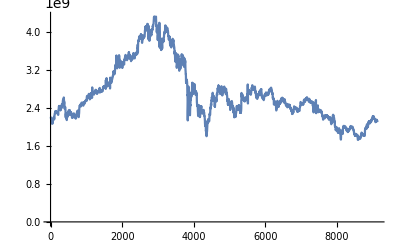

```mathematica
ListLinePlot[twapsWethUsdc90dFiltered, PlotRange->All]
```

```mathematica
FromUnixTime[tblWethUsdc90d[[40]][[2]]]
```

Mon 19 Apr 2021 17:14:44GMT-4.

```mathematica
FromUnixTime[tblWethUsdc90d[[Length[twapsWethUsdc90dFiltered]]][[2]]]
```

Wed 30 Jun 2021 04:33:51GMT-4.

```mathematica
(* Calculate the rs ... *)
```

```mathematica
rsWethUsdc90dFiltered = Differences[Log[twapsWethUsdc90dFiltered]]
```

{-0.00120673,0.000176452,-0.0000603568,-0.000373722,-0.000389599,0.000559858,-0.00092094,-0.00154871,-0.000905547,-0.000584311,-0.00172231,-0.00371162,9115,0.00150055,0.000591025,0.000421125,-0.000241228,-0.000868266,-0.00297129,-0.00294238,-0.00298715,-0.00213101,-0.00225849,-0.00116666}
 |  |  |  |

```mathematica
rsWethUsdc90dFiltered[[100]]
```

-0.00443888

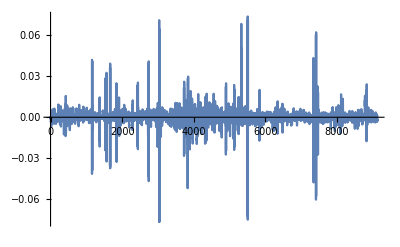

```mathematica
ListLinePlot[rsWethUsdc90dFiltered, PlotRange->All]
```

```mathematica
edistWethUsdc90dFiltered = EstimatedDistribution[rsWethUsdc90dFiltered, StableDistribution[1, aWU90d, bWU90d, locWU90d, scaleWU90d]]
```

StableDistribution[1,1.46465,-0.0496207,-0.000010553,0.00154277]

```mathematica
(* This seems more reasonable. more data from weth/usdc lead to decrease in alpha because included massive run up to $4k *)
```

```mathematica
FromUnixTime[tblWethUsdc90d[[5000]][[2]]]
```

Fri 28 May 2021 06:16:07GMT-4.

```mathematica
FromUnixTime[tblWethUsdc90d[[Length[tblWethUsdc90d]]][[2]]]
```

Wed 30 Jun 2021 12:09:58GMT-4.

```mathematica
(* Compare with last month which should be close to same fit as ethDai above *)
rsWethUsdc90dFilteredLastMo = Table[rsWethUsdc90dFiltered[[i]], {i, 5000, Length[rsWethUsdc90dFiltered]}]
```

{0.00138357,-0.000502391,-0.0008089,0.000653862,0.000838998,0.00220502,0.00321165,0.00330788,0.00117512,-0.000562798,-0.00197869,-0.00183754,-0.00199201,-0.000535229,-0.00218048,-0.0042712,-0.00534709,-0.00989363,-0.0138703,-0.00788287,-0.00782501,-0.00459214,-0.00146182,0.00367574,-0.000613387,0.00198114,0.00132682,0.00062465,0.00173689,0.00252148,0.00330751,0.00314845,0.00184518,0.00416517,0.0038529,0.00237258,0.00373025,0.00770687,0.00542132,0.00638319,0.00649788,0.00348426,0.00135944,0.00037847,-0.00129262,-0.00164407,-0.00094984,-0.000819793,-0.000817573,-0.000115755,0.00215873,0.00118038,0.000974682,0.000611831,0.00114596,-0.00133368,-0.000508815,-0.000644953,-0.00291971,-0.00348848,0.00186567,0.00265191,0.00265224,0.00480574,0.00579584,0.00103365,-0.000509407,-0.000330017,-0.000495765,-0.00127583,-0.00211673,-0.00204222,-0.00167189,-0.00394297,-0.00133476,-0.00437399,-0.00368055,-0.00363791,-0.00298446,-0.00207732,-0.00368578,-0.0040298,-0.00374721,-0.0039401,-0.00241761,-0.00194952,-0.000122209,0.0000707798,0.00125222,0.000158842,-0.000113324,-0.000534232,-0.00103567,-0.00232923,0.000967507,0.00148154,0.0021478,0.00149676,0.00243626,-0.00204814,-0.00267195,-0.00494095,-0.00288642,-0.00391347,-0.00398112,-0.00435899,-0.00301742,-0.000779682,0.00415815,0.000962671,0.000860287,0.010136,-0.0110061,-0.00830702,-0.00568145,-0.00420214,-0.0159207,0.00921851,-0.00261105,0.000380373,0.00144039,0.00260625,0.00350121,0.00334364,0.000274729,-0.00195733,-0.00504269,-0.0080455,-0.00725023,-0.00563314,-0.00399463,-0.00191707,0.0236429,-0.0239422,0.000414774,-0.00307299,-0.00284132,-0.0216168,0.0203976,-0.00226333,-0.000437824,-0.00166712,-0.00285656,-0.00182893,0.00186321,0.00146714,0.000697305,0.00245018,0.00265946,0.00198315,0.00153379,0.00234511,0.00205597,-0.000385992,-0.00115037,0.000515103,0.00107707,0.00185109,0.00404967,0.00177961,-0.0000155981,-0.00412897,-0.00607348,-0.00982657,-0.00707735,-0.00265576,-0.00145168,-0.000582316,0.00100444,0.0000795083,-0.0011279,0.000412785,0.00287009,0.0038199,0.00466839,0.00384655,0.00301581,0.00523719,0.00399675,0.0014789,0.000814174,0.00149761,0.0011321,-0.0010015,0.000565912,0.00232665,0.00116676,0.000989664,0.00349766,0.00499907,0.00369757,0.00484502,0.00647648,0.00581668,0.00510051,0.00346726,0.00285234,0.00376861,0.00309614,0.00287301,0.00151973,0.00188457,0.00250909,0.0014385,0.00191065,0.00135052,0.00102274,-0.00103342,-0.00140558,-0.00218777,-0.00084068,-0.0000911912,-0.00035525,-0.000919487,-0.000609882,-0.000764191,-0.00123952,-0.00229446,-0.000407143,-0.000360759,-0.00137499,-0.000234925,0.000510127,-0.000504314,-0.000656455,0.00153131,0.00284109,0.0025525,0.00145296,0.00183079,-0.00169771,-0.00515199,-0.00494981,-0.00293253,-0.00260132,-0.00179628,-0.000120559,0.000359513,-0.000658332,-0.00283448,-0.00286926,-0.00229154,-0.00259539,-0.00181111,0.0000962952,0.000725821,0.000398363,0.000991748,0.00203276,0.00183962,0.00366163,0.00480021,0.00160922,0.00267489,0.0028054,-0.0123434,0.0146261,0.00168937,0.0021605,0.00156252,0.014717,-0.0117672,0.00231614,0.0024634,0.0020107,0.00137728,0.00027797,-0.000606795,-0.000857535,-0.00161363,-0.00173191,-0.000141334,-0.000162723,-0.000430384,-0.000107299,-0.00019521,-0.00195787,-0.000377088,-0.000435901,-0.000854876,-0.000249213,-4.52375×10^-6,-0.0018833,-0.00281351,-0.00106577,-0.00278537,-0.00328394,-0.00115053,-0.00141462,-0.00197525,-0.000762788,0.000711764,-0.00178419,-0.00329936,-0.00212328,-0.00244367,-0.00415163,-0.00301704,-0.00258962,-0.00322915,-0.0041276,-0.00501461,-0.00292997,-0.00257462,-0.000614709,0.000136798,0.00150618,-0.000734772,-0.000279531,0.000315429,-0.000675488,-0.00219989,0.00116628,0.000868744,-0.00106751,-0.000403647,0.00036552,0.000286648,0.000169577,0.00164569,0.00253414,0.00206007,0.00195932,0.00133675,0.00223121,0.00221616,0.0029065,0.00321967,0.00454456,0.00572462,0.00610639,0.00654602,0.0682849,0.00151787,0.00131724,0.00131024,0.00112468,0.0503312,-0.00246866,-0.00423772,-0.00370747,-0.00475171,-0.00613171,-0.00333521,-0.00258475,-0.00244691,-0.0015985,0.00267089,0.00232105,-0.000253034,-0.00115857,-0.000797331,-0.00278088,-0.00179448,0.000554381,0.00174845,0.000996153,0.00151432,0.00237329,0.00177267,0.00374535,0.00435367,0.00408662,0.00074626,-0.00141383,-0.00223213,-0.0045066,-0.00242413,-0.00157254,-0.000934367,-0.00082802,-0.000598762,-0.00201921,-0.00346327,-0.0041836,-0.00610033,-0.00623173,-0.00522788,-0.000643148,-0.00136907,-0.000752326,0.000226207,-0.00039746,-0.000547424,0.00138937,0.002254,0.00272656,0.00242767,0.00192893,0.00116984,0.00197335,0.00181781,0.00182954,-0.000225958,-0.00216422,-0.00309368,-0.0031119,-0.00393579,-0.00405658,-0.00340455,-0.00102049,0.00293076,0.00466791,0.00620655,0.00716569,0.00301632,-0.00049342,-0.00183915,-0.00262493,-0.00481624,-0.00333266,-0.00361344,-0.00397059,-0.00152033,-0.000997983,-0.000387262,0.000223988,0.000443175,-0.000812935,-0.00152526,-0.00167601,-0.00253996,-0.00213284,-0.000272701,0.00104264,0.00153179,0.00195502,0.00187094,0.00177268,0.00139028,0.0000605359,-0.00061421,-0.000716065,-0.00236212,-0.00264026,-0.000879422,-0.000690278,0.000427604,0.00189638,0.00203956,0.00770315,-0.00470943,0.00200956,0.00110936,0.000668517,-0.00436758,0.00801729,0.00183594,0.00107399,0.00107966,-0.000589933,-0.000738892,-0.000778657,0.00103232,0.00301867,0.00425626,0.00331123,0.00234433,-0.00137603,-0.0017703,-0.00207169,-0.00305418,-0.0039642,-0.00371719,-0.00252594,-0.00307525,-0.00083348,0.00163672,0.0025243,0.00311782,0.00287412,0.00275,0.00137232,0.00224385,0.00174039,0.00120751,0.000765431,0.00110704,-0.000302941,-0.0000705755,0.000473032,0.00111129,0.0007566,0.000265303,-0.00044658,-0.00101858,-0.000949514,-0.000495734,0.000383648,0.00147085,0.00177237,0.00171421,0.00148599,0.000540162,-0.0103462,0.0104284,0.00138477,0.00203147,0.00427145,0.0143392,-0.00692159,0.00181754,0.00131586,-0.000406964,3.85083×10^-6,0.000599227,0.00132476,0.000962741,0.000505646,0.000164573,-0.000552177,-0.00124142,0.0737268,-0.0749103,-0.000178554,-0.000648149,-0.000594988,-0.0725458,0.0710715,-0.000703423,0.000635076,0.0012459,0.00139657,0.0024652,0.00179055,0.000972723,0.000453187,-0.000156787,-0.000929172,-0.000170599,0.00205953,0.0017503,0.00354047,0.00243561,0.0024765,0.00015919,0.00123097,0.00230305,0.00293316,0.00330839,0.00405037,0.0011382,0.00199529,0.0013113,0.0000884439,0.000186293,-0.00140584,-0.00180634,-0.00143473,-0.00140722,-0.00208754,-0.00218291,0.000266358,0.00039906,0.000711173,0.000366808,0.000503414,0.0000597492,3.38456×10^-6,-0.00013065,0.000297545,-0.0000625496,-0.000335263,-0.0000659065,-0.000449077,-0.00112177,-0.00222992,-0.00199153,0.000842701,-0.0058487,-0.00153716,-0.000651958,-0.000353654,-0.00413394,0.00354431,-0.000251926,-0.000394835,-0.0012019,-0.00209312,-0.00255229,-0.00178315,-0.00205506,-0.0011223,0.00147551,0.00196756,0.00111173,0.00146489,-0.000942578,-0.000664131,-0.00104557,-0.00093927,-0.000431669,0.000665416,0.000457847,0.0000571973,-0.000522239,-0.00233493,-0.00119945,-0.00173565,-0.000788789,0.0000891099,0.0020079,0.00185253,0.00147588,0.00291102,0.00256705,0.00264791,0.00185552,0.00226623,0.00487222,0.0032551,0.00342489,0.00284003,0.0034957,0.00345195,0.00314135,0.00157276,0.001643,0.00245114,0.00207552,0.00218316,0.00151575,0.000734518,-0.000630349,-0.000982388,-0.00214893,-0.000435571,0.000501004,0.00117267,0.000938933,0.00150384,0.000892152,0.00134826,0.00123052,0.000865619,0.00269673,0.00298819,0.00262722,0.00237609,0.00121555,0.00145949,-0.000956662,-0.00295379,-0.00347422,-0.00251992,-0.00331122,-0.00530656,-0.00376684,-0.00213397,-0.0019975,-0.000606032,0.00205911,0.00298467,0.00146204,-0.000197428,-0.00184902,-0.00376908,-0.00367447,-0.00251604,-0.00253455,-0.00101702,0.000249013,0.0002988,0.000632265,0.00160092,0.00116486,0.00131658,0.0000962287,-0.00113252,-0.000776909,0.000259244,0.000641181,0.00319794,0.00305452,0.00277978,0.00214586,0.00150175,0.000794801,0.000163936,0.000246373,0.0000895209,-0.000928167,-0.00216834,-0.00181197,-0.00253857,-0.00189043,-0.00286676,-0.00148391,-0.000564698,-0.00027703,-0.0000892077,0.000365188,0.000463784,0.000613771,0.000697667,0.000961774,0.00178805,0.00255678,0.00232866,0.00137599,0.00116704,-0.000317344,-0.000508354,-0.0000920877,0.00113555,0.00100884,0.00125818,0.00100572,0.00117365,0.00296527,0.00142948,0.000343872,-0.00140287,-0.00229742,-0.003995,-0.00378926,-0.00278027,-0.00469043,-0.00415918,-0.00615643,-0.0051435,-0.00661826,-0.00377184,-0.00290893,0.000715451,0.000418536,0.000218857,0.00184398,0.00148775,0.00273642,0.00204957,0.00123504,0.00230034,0.000538156,-0.00114434,-0.00154688,-0.00154699,-0.00284655,-0.00391952,-0.00392474,-0.00611048,-0.00478061,-0.00487846,-0.00218003,-0.00224164,-0.000945058,-0.00279071,-0.00357163,-0.00459777,-0.00421826,-0.00176876,0.000509433,0.000353261,0.00103143,0.00173099,0.000493948,0.000572196,0.000939899,-0.000264109,-0.000200109,-0.000295463,0.00019208,0.00133795,0.00265068,0.00254559,0.00126911,-0.0000476691,-0.000522026,-0.00162218,-0.00141526,-0.00102138,-0.000447212,-0.000601125,-0.0006671,-0.00551583,-0.00382775,-0.00384136,-0.00160833,0.00200902,0.0058714,0.0044515,0.00587412,0.00302359,0.000819265,0.0000963087,-0.000572638,-0.00290529,-0.00273559,-0.00172571,-0.000282459,0.00120951,0.0016928,0.0014632,0.00138092,0.000752905,0.0011534,0.00229917,0.00216595,0.00133041,0.00103479,0.000150951,-0.000870348,-0.0000400718,0.00214633,0.00327525,0.00288026,0.00210891,0.00124842,-0.000544242,-0.000973308,-0.000497529,0.000378602,0.00108602,0.000683532,0.000343748,-0.000509143,-0.00145384,-0.00149724,-0.000810789,-0.000469049,0.000374332,0.001392,0.000937522,0.00230366,0.00253887,0.00200202,0.00274825,0.00154487,0.000696153,-0.000200479,-0.000484026,-0.000215671,0.000368268,-0.000188988,-0.00110843,-0.0040895,-0.0035981,0.0120268,-0.0171511,-0.00145302,0.00340849,0.00357518,-0.0114071,0.0200212,0.00548388,0.00423795,0.00218627,0.00117478,0.00070182,0.000449259,0.000263951,0.000174885,0.000257494,-0.000657243,-0.00103309,-0.000778653,0.000155191,0.000897793,0.000504912,0.000683158,0.000302899,-0.000117403,0.000126242,0.000339236,0.000365681,0.000861902,0.000441948,0.00102859,0.000523017,0.000346992,-0.00056147,-0.000646079,-0.00134424,-0.000352915,0.0000939858,0.000894328,0.000703523,0.000560131,0.00034389,0.00108238,0.00200825,0.00209228,0.00171306,0.000395213,-0.000621728,-0.000886851,0.000084524,0.000634543,0.00123931,0.00116906,0.000775816,-0.000125214,-0.00421532,-0.00758927,-0.00708203,-0.00619416,-0.00506499,-0.00286216,-0.00022942,0.000397763,-0.00228203,-0.00284739,-0.0037728,-0.00491159,-0.00621204,-0.00360361,-0.00237526,-0.00154884,0.0000910636,0.000660443,-0.000672592,-0.000234471,-0.000930915,-0.000821889,-0.000976592,-0.00106184,-0.00113873,-0.0010292,-0.000469048,-0.00185339,-0.00128201,-0.00158866,-0.000753845,-0.000315131,0.00333583,0.00389832,0.00320227,0.00164615,0.000978823,-0.000856096,-0.00161876,-0.00137609,-0.000734265,-0.000807374,-9.53827×10^-6,-0.000251205,-0.0000757944,-0.0000675668,-0.0000362852,0.000115731,0.000420212,0.000468732,0.000212061,0.000238146,0.0000676835,-0.000781357,-0.00120201,-0.000196939,-0.000663745,-0.000172342,0.000461309,0.00155729,-0.0000383186,-0.00138066,-0.0043719,-0.00461817,-0.00549591,-0.00281956,-0.0033277,0.000931298,0.00101437,0.00124075,0.000634,0.000960407,0.000778599,0.000918206,0.00227385,0.00277604,0.00231648,0.00263451,0.00323809,0.00208864,0.000553065,0.00063431,0.00251325,0.00248606,0.0025885,0.00301162,0.00263541,0.00247708,0.00161572,0.00168183,0.00126436,0.000459245,0.0000147376,-0.000946088,-0.000990665,-0.000830413,-0.0008201,-0.000291875,0.000455742,0.000492238,0.00062987,0.000581815,0.000472264,0.000113498,0.0000203107,-0.000248606,-0.000109342,6.11874×10^-6,0.000744982,0.0011467,-0.000722883,-0.00166837,-0.00138068,-0.00182956,-0.00237018,0.0000893746,0.0012614,0.00147661,0.00200309,0.00235084,0.00316252,0.00276495,0.00167301,0.00208137,0.00242818,0.00157317,0.00156372,0.00136751,0.000949486,-0.000479218,-0.000871039,-0.000934996,-0.00141415,-0.00149613,-0.000776058,-0.000998857,-0.00114118,-0.000342696,-0.000148621,-0.00129264,-0.000820701,0.000540971,-0.000141961,-0.000278254,-0.00017462,-0.000104798,-0.00206535,-0.00221242,-0.00131605,-0.00311589,-0.00259081,-0.0011853,0.0000274467,0.000246535,0.00143296,0.00385469,0.00421111,0.00336976,0.00363197,0.00151883,0.000643588,0.00050146,0.000646639,0.000321336,0.00066608,0.000304966,-0.000601686,-0.000901216,-0.00151989,-0.00143568,-0.0026651,-0.00182229,-0.00199269,-0.000980007,-0.000887543,-0.000361201,-0.000338609,-0.000416367,-0.000319939,-0.000523584,-0.000468607,-0.000285406,-0.000725099,-0.000664394,0.0000121163,-0.0000292065,0.00105458,0.00127579,0.002435,0.001434,0.00254895,0.000806306,0.000276946,-0.000118753,-0.0014241,-0.00179643,-0.00198118,-0.00118081,-0.000113633,0.000271651,0.00132062,0.00143175,0.00127808,0.000940566,0.00260845,0.00347682,0.00299882,0.00391286,0.00396371,0.00134539,0.000896086,0.000792952,0.00173315,0.00118305,0.00186588,0.00330538,0.00234282,0.00112744,0.000688898,0.000195579,0.0004659,-0.0000885517,-0.0011934,-0.0019336,-0.00177465,-0.000973092,-0.000205586,0.000130158,0.000520508,0.000723474,-0.000631636,-0.000511002,-0.000128511,-0.000170918,0.0000418053,0.000458622,0.000487467,0.000388524,0.000415511,-0.0000748334,-0.00129561,-0.00228951,-0.00191005,-0.00220365,-0.000993657,-0.000259343,0.000743477,0.0011043,0.000154635,-0.000347806,-0.0000253046,-0.000265925,-0.000261337,0.000902791,0.00164145,0.00151965,0.00240736,0.00317069,0.00277716,0.00278098,0.00361281,0.00382874,0.00133969,0.000429014,-0.000219775,-0.000603586,-0.00107425,-0.00107175,-0.000988601,-0.00108339,0.00044718,0.00125588,0.00156303,0.00215731,0.00128198,-0.00133692,-0.00194093,-0.00235805,-0.00397652,-0.00292992,-0.00163381,-0.00231365,-0.00226288,-0.000939374,-0.000707856,-0.000392733,0.000363077,0.000891722,0.000316821,0.000536812,-0.000136659,-0.000970526,-0.000966996,-0.000752043,-0.00160942,-0.00278919,-0.00312601,-0.00239856,-0.00329212,-0.00221399,-0.00151277,-0.00264654,-0.00183216,-0.00129921,-0.00189073,-0.00220761,0.0000904129,-0.000642222,0.000396686,0.00161633,0.00253884,0.00217108,0.00169264,0.000387029,-0.000795113,-0.00438286,-0.00520797,-0.0076173,-0.00908248,-0.00714884,-0.00492997,-0.00350887,0.000869211,0.0020181,0.000900393,0.00100446,0.000919799,-0.00038259,-0.000746017,-0.00112199,-0.00093847,-0.00217957,-0.00242573,-0.000970018,9.73713×10^-7,-0.00204876,-0.00127317,-0.000956699,-0.000433515,0.000249671,0.00214142,0.00212519,0.00171571,0.000354234,-0.000819808,-0.000354395,-0.00128662,-0.00538522,-0.00834931,-0.00906963,-0.0100541,-0.00903637,-0.00523068,-0.00105636,0.00172766,0.0037,0.00395243,0.00249004,0.00112561,0.000296208,-0.00107279,-0.00115422,-0.00253738,-0.00222511,-0.00117596,0.0000214833,-0.000374061,0.00111911,0.000964661,-0.000320662,-0.00259509,-0.00128712,0.00148615,0.00190801,0.00185944,0.00323821,0.00411713,0.00275917,0.00204674,0.00342977,0.00237256,6.75497×10^-6,-0.00175446,-0.00281844,-0.00432686,-0.00372338,-0.0021735,-0.000155976,0.000894364,-0.000183997,-0.000375917,-0.000384655,-0.0014041,-0.00131397,0.00130801,0.00111892,0.0018494,0.00282388,0.00161329,0.00729787,-0.00434497,-0.000237511,-0.00176389,-0.0013761,-0.00908489,0.00241441,-0.00221657,-0.00290881,-0.0041856,-0.00660246,-0.00823313,-0.00659426,-0.00763719,-0.00572171,-0.00320274,-0.00462218,-0.00519939,-0.00395445,0.000268787,0.00113391,0.00645951,0.00645686,0.00545902,0.00286797,0.000932358,-0.000470184,-0.000528784,-0.000601199,-0.000343658,0.00053873,0.00117019,0.00334946,0.00393247,0.00419288,0.00525311,0.0039867,0.00250459,0.00163644,0.00157629,0.0021982,0.00145962,0.00158184,0.00192577,0.00229886,0.00192283,0.00392012,0.00332524,0.00257608,0.00212244,0.000201313,-0.00100292,0.0104538,-0.0120182,0.0000949793,0.00037985,0.00118448,-0.0116273,0.0116724,0.000294076,-0.000178225,-0.000922559,-0.000635898,-0.000700783,-0.00242206,-0.00356008,-0.00353252,-0.00316181,-0.00410936,-0.0033285,-0.00180118,-0.000870154,-0.00151985,-0.0015235,-0.0019408,-0.00195803,-0.00256734,-0.00309712,-0.000065354,0.0016948,0.00105554,0.00261928,0.00282118,0.000667051,0.000773186,-0.000151264,-0.00252705,-0.00332367,-0.00195226,-0.00235918,0.000158523,0.00317528,0.00515721,0.00386567,0.00411899,0.00188634,0.000969425,0.000769984,0.00202387,0.00415562,0.00385459,0.00504629,0.00265851,0.000508702,0.000174222,-0.000864294,-0.00322233,-0.00232551,-0.0018504,-0.00249754,-0.0023831,-0.000828802,-0.00139631,0.000127146,0.000497937,0.000713045,0.000241475,-0.00019934,-0.00107581,0.0000943279,0.00123469,0.00133947,0.0013753,0.00124376,0.000328516,-0.000349706,0.0020011,0.00558366,0.00467831,0.00487386,0.00382893,0.00116768,-0.00192066,-0.00222065,-0.00211705,-0.00233435,-0.00171002,-0.000818518,-0.0000364249,-0.000759544,-0.000590536,-0.00058998,-0.00375499,-0.00160057,0.00115487,0.00382678,0.003931,0.0064611,0.00471153,0.00201578,0.00128854,0.00242407,0.00280464,0.00287481,0.00278257,0.00186848,-0.000473112,-0.00183432,-0.000739916,-0.00198568,-0.000625336,-0.00130265,-0.000481152,-0.00138739,-0.00216007,-0.0021429,-0.000984917,-0.00107414,-0.000329693,-0.00065146,-0.000192942,-0.0000257997,0.000280241,0.000444493,0.000150389,0.000204397,0.00079291,0.00139836,-0.00382732,0.00811122,0.00367767,0.00210771,0.0013822,0.00733195,-0.00581892,-0.000805843,-0.000520799,-0.00063499,0.000177683,-0.0101817,0.0098592,-0.00105081,-0.00103771,-0.00125053,0.00943614,-0.0112429,0.000678369,0.000927984,0.000567046,-0.000437418,-0.000225454,-0.00326811,-0.00210294,-0.00198096,-0.000594954,0.000116189,0.000785527,0.00162587,0.00138752,0.000510806,-0.000409311,-0.00118884,-0.00165245,-0.00161874,-0.00215621,-0.00173664,-0.00123015,-0.00148931,-0.00208647,-0.00144291,-0.00129503,-0.00114748,-0.00165525,-0.000403278,0.000391071,0.00054959,0.000574187,0.000691054,0.00101729,0.000838899,0.000417738,0.000534281,0.000349994,0.0000784903,-0.000627681,-0.000338264,-0.00181361,-0.00233764,-0.00172327,-0.00315139,-0.00181947,0.00138678,0.00290388,0.00420467,0.00615782,0.00634208,0.00495199,0.00255745,0.00110843,-0.000227538,-0.000930363,-0.00195546,-0.00182955,-0.00190961,-0.0012198,-0.00166061,-0.00212553,-0.00158387,-0.00119889,-0.000707689,-0.000517388,-0.000289131,-0.000508175,-0.00105978,-0.00107777,-0.000866398,-0.00114392,-0.00103948,-0.00132233,-0.00184714,-0.00171039,-0.000824872,-0.00053943,-0.000199978,-0.000652229,-0.00120717,-0.00230521,-0.00245851,-0.0027843,-0.00152617,-0.00221123,-0.00118026,-0.00158777,-0.00204787,-0.00169918,-0.000987628,-0.000791995,0.00042513,0.000595238,0.0000912668,-0.000200082,-0.000261872,0.0000834129,-0.000367272,-0.00073548,0.000104366,0.0000763078,-0.00122581,-0.002011,-0.00213668,-0.00227274,-0.00104558,0.000769176,0.0016978,0.00324041,0.00253123,0.00119172,0.00115975,0.0015242,0.00150696,0.00112335,0.000993403,0.00137758,0.000973588,0.000409752,0.000360809,0.000423089,-0.000902948,-0.00240677,-0.000363357,-0.00159372,-0.00240626,-0.00270044,-0.00251929,-0.00588602,-0.00486438,-0.00314804,-0.00212106,-0.000777348,0.00012803,-0.0000803099,0.0000158108,0.000327033,0.0000585264,0.00169697,0.00392655,0.00418031,0.00276579,0.00278992,0.00123728,0.000759748,0.000139934,0.000483833,0.00120233,0.000996408,0.00120538,0.00109166,0.00117945,0.000192361,-0.0000758085,-0.00089945,-0.00162417,-0.00243287,-0.00241437,-0.00190366,-0.00298,-0.00270134,-0.00196889,-0.000728597,0.000108256,-0.000105529,0.00169702,0.00243526,0.00180384,0.000929291,0.00175859,0.000364797,-0.000387275,-0.000146197,0.000515033,0.000741775,0.000986732,0.00132487,0.00106733,0.000183471,0.000741398,0.000985236,0.000727342,0.000373811,-0.0000794104,-0.000610078,-0.000381819,-0.000856791,-0.000770829,-0.00113646,-0.000902991,-0.000663444,-0.000974004,0.000132717,0.000708582,0.000808384,0.00113019,0.000586468,0.00129185,0.0000247615,-0.000260407,-0.000740653,-0.000777433,-0.00190253,-0.00234654,-0.00299916,-0.00351023,-0.00310979,-0.00315303,-0.00163215,-0.000523491,-0.00223963,-0.00331267,-0.00311477,-0.00333986,-0.00263423,0.0000789393,0.00166717,0.00187448,0.00188498,0.00118253,0.000244067,-0.00063535,-0.000358262,0.000449735,0.000726013,0.0010777,0.00163898,0.000773039,-0.000272121,-0.00104508,-0.000699654,-0.000720447,-0.000755901,-0.000495187,-0.00172287,-0.0017866,-0.00310014,-0.00616721,-0.00436799,-0.00261539,-0.00224186,0.000346961,0.00238863,0.00197832,0.00157715,0.000505562,-0.00222257,-0.00300158,-0.00214269,-0.000985974,-0.000489342,0.000662812,0.000615882,-0.000113019,-0.00102186,-0.000959408,-0.000435733,0.000154946,-0.00237619,-0.00311633,-0.00318059,-0.00418648,-0.00538427,-0.00359328,-0.00235378,-0.00190942,-0.00142651,0.00123368,0.00278863,0.000376521,0.000414409,0.00164757,0.000705796,-0.000175621,0.000878569,0.000330923,-0.00120537,-0.00154788,-0.000802105,-0.000303097,0.000705601,0.00039071,0.000572838,0.0000186143,0.000186461,0.000111658,0.0000638506,0.000646659,0.00193114,0.00153203,0.00211789,0.00244784,0.0020981,0.00016032,0.000085974,0.000136234,-0.000122241,-0.00038779,-0.000467547,0.000118102,0.000258345,0.000372335,0.000597151,0.00104895,0.000693994,-0.00051614,0.00344653,0.0057179,0.00549318,0.00464513,0.00654503,0.00188217,-0.000547873,-0.000422434,-0.000043949,0.00165629,0.00293781,0.00513118,0.00433745,0.0045191,0.00269509,0.00157889,0.0000995733,-0.000191876,-0.0000833281,-0.00113714,-0.00174032,-0.00196257,-0.00149424,-0.00120482,-0.0000214462,0.00044028,0.000149757,0.000197957,-0.00272666,-0.00215284,-0.00245966,-0.00175965,-0.000527626,-0.00251589,-0.00108841,0.000283313,0.000184764,0.000209911,-7.57875×10^-6,0.0000290462,0.0000541132,0.000254002,0.000429459,0.00214266,0.00215318,0.00161292,0.00128743,0.00128104,-0.000199107,0.000557158,0.000627845,0.000599131,0.000579566,0.00032921,-0.000132388,-0.000310325,-0.000393885,-0.000444571,-0.000080268,-0.000349965,-0.000270326,-0.000887906,-0.000606425,-0.000805393,-0.000784103,-0.000849789,0.0000183833,-0.000478711,-0.00147757,-0.00179449,-0.00220053,-0.00174439,-0.00198671,-0.0000477245,0.000220608,0.000481677,-0.000436369,-0.00106316,-0.00204256,-0.00109954,-0.00297412,-0.000317153,0.00264747,0.0039027,0.00291522,0.00431977,0.00264004,0.000777574,0.000165431,0.00017485,-0.0000973408,-0.000269611,-0.0010164,-0.00188691,-0.00298119,-0.00374135,-0.00604915,-0.00471184,-0.00408054,-0.00297962,-0.00199183,-0.0000848946,0.000414396,0.000408973,0.000319172,-0.000274525,-0.0015854,-0.00110331,-0.00137174,-0.00120193,-0.000819512,-0.000446821,-0.000392834,-0.000281157,0.00051284,0.00144365,0.00141921,0.0018823,0.00105642,0.000654523,-0.000383039,-0.000583754,-0.000917324,0.00057479,0.00195792,0.00198205,0.00202801,0.00187692,0.000861388,-0.000588349,0.0000557887,0.000465782,0.000698376,0.000956501,0.00172077,0.00100012,0.00129233,0.000482502,0.000594177,0.000160617,-0.000173,-0.000688544,-0.00046369,0.00029861,0.000527998,0.0000667645,0.000276601,0.000164544,-0.001586,-0.00199479,-0.000978729,-0.000724394,-0.000653827,0.00033314,0.000303816,-0.000583703,-0.0014229,-0.00140908,-0.00158961,-0.00166357,-0.000747297,0.00010177,0.0000682732,0.0000740827,0.000455547,0.000726368,0.00270792,0.00429226,0.00456719,0.00371084,0.00442128,0.00186139,0.000831423,0.00124536,0.00106012,0.00146182,0.00275312,0.00299018,0.00237153,0.00231828,0.00131176,0.00132583,0.000450654,-0.0011882,-0.000401531,-0.000167336,-0.000155508,0.00147783,0.00440459,0.00403828,0.00448504,0.00620618,0.00523114,0.00311099,0.00332931,0.00316907,0.00290075,0.000665313,-0.0000917766,-0.000594179,-0.00133941,-0.00157606,-0.0012642,-0.0027633,-0.0011194,-0.000563164,-0.000374505,-0.000522978,-0.000361378,-0.000677285,-0.000386873,-0.00033102,-0.000734773,0.000113981,0.0000222537,0.000524375,0.000669797,0.000346092,0.000408195,0.000405554,-0.000194319,-0.000719825,-0.000247964,-0.000412707,-0.000435787,-0.000490027,-0.00141669,-0.00205273,-0.0021157,-0.00188434,-0.00153977,-0.0000618899,0.000941715,0.000781004,0.000539564,0.000515963,0.000316346,0.000795668,0.00151319,0.00165739,0.00126897,0.00116286,0.000171823,-0.000335948,-0.000359767,-0.000295686,0.000157154,0.000322547,0.000243427,0.000151183,-0.0000257181,-0.000464895,-0.00124161,-0.00145442,-0.0014681,-0.00156599,-0.000931468,-0.00014052,-0.000240283,-0.000180602,-0.0000759411,-0.000436969,-0.000637627,-0.000704452,-0.000240754,0.0000655584,0.00146486,0.00163005,0.00153055,0.000722157,0.000295732,-0.00085708,-0.000718137,-0.000776849,-0.000425826,-0.000536857,0.000151933,0.0004261,0.00130226,0.00316072,0.00352088,0.00515082,0.00477228,0.00542246,0.00239447,0.00249542,0.00266166,0.00145438,0.000999162,0.000407197,-0.000319321,-0.00100556,-0.00123837,-0.00145694,0.000202911,0.00191656,0.00251958,0.00304072,0.00198181,0.000180017,-0.000712801,-0.00140474,-0.00212404,-0.000190435,0.000122504,0.0001267,0.0000583374,-0.000012132,-0.000251298,-0.00111739,-0.00272137,-0.00245011,-0.00390432,-0.00328688,-0.00181335,-0.000465326,-0.000575833,0.00122654,0.000987185,0.000095763,0.0000525689,0.000599119,0.00170057,0.00181482,0.00178389,0.00182087,0.00195773,0.000243611,0.00021536,0.00017933,0.000355814,2.77846×10^-6,-0.0000471764,-0.00012278,0.000180821,0.000477659,0.000540327,0.00141695,0.00132348,0.00187454,0.00180777,0.00354874,0.00344521,0.00197666,0.000582299,-0.000990836,-0.00128793,-0.00160008,-0.00177255,-0.00199202,-0.00150616,-0.000598593,-0.000338292,0.000361398,0.00159628,0.00104458,0.000381642,0.00022685,0.000284647,0.000219794,-0.0000114379,-9.00831×10^-6,0.000669606,0.00140921,0.00280739,0.00304181,0.00278891,0.00177603,0.000491838,-0.000646235,-0.000910519,-0.000532737,0.00016117,0.000591572,0.000509347,-0.0000211151,-0.000435457,-0.000882013,-0.00149794,-0.00127846,-0.000608128,-0.000148474,0.000256831,0.000564216,0.000693336,-0.000349317,-0.00177616,-0.00270576,-0.00340488,-0.00340829,-0.00126883,0.000292087,0.000439381,0.00103597,0.000475984,-0.000269776,-0.000410265,-0.000261725,-0.00027354,-0.000220558,-0.000108141,-0.000395803,-0.000638836,-0.000531092,0.000252769,0.000853727,0.00121233,0.00107895,0.00114832,0.000506637,0.000212304,-0.000112601,0.000460984,-0.0000376302,-0.00043204,-0.00122866,-0.00190194,-0.00349229,-0.0029311,-0.00298528,-0.00237405,-0.00200858,-0.000837997,-0.000614386,-0.00083808,-0.000097026,0.000363564,0.000492928,0.000564801,0.000594756,0.000837353,0.00150263,0.000778056,0.000734278,0.000728584,0.00158337,0.00347977,0.00323427,0.00308572,0.00197221,0.00152131,-0.00265093,-0.00201048,-0.00287649,-0.0040997,-0.00237566,-0.00500968,-0.00311829,-0.00312649,-0.00210574,-0.000507067,-0.000258394,0.000313206,0.000165185,-0.0000949122,0.000162786,0.000136349,0.000249247,0.000687187,0.00106854,0.00157711,0.00171695,0.00193276,0.00161207,0.00149536,0.0012551,0.000301446,-0.00117422,-0.00216294,-0.00217996,-0.00240103,-0.00229972,-0.00118411,-0.00084814,-0.00171898,-0.00105637,-0.00129531,-0.00124298,-0.00011673,0.000854595,0.000995375,0.00135413,0.00042574,0.000503852,0.000558207,0.000111085,-0.000285399,-0.000491212,-0.000594052,-0.000534638,-0.000332045,-0.000236989,-0.0000233016,0.000114342,0.000617067,0.000701093,0.00109654,0.000875183,0.000733453,0.000292417,-0.000185182,-0.000148921,-0.000325314,-0.000163453,-0.0000902933,-0.0000855103,-1.02944×10^-6,0.000262285,0.00166389,0.00135023,0.00142386,0.000831886,0.00124945,-0.000792387,-0.00077216,-0.000723545,-0.000869719,-0.00114805,-0.000574998,-0.000911931,-0.000975607,-0.0006243,-0.000712944,-0.000455549,-0.00100024,-0.000389541,-0.000708389,-0.00205415,-0.00329259,-0.00269561,-0.00314314,-0.0039649,-0.00311602,-0.00247075,-0.00209872,-0.00100563,-0.0013449,-0.000977663,-0.0010642,-0.000322535,-0.000327992,0.000843122,0.00123011,0.000670844,0.000426698,0.000220492,-0.000569701,-0.00121417,-0.000838284,-0.00222869,-0.00237405,-0.0029726,-0.00220274,-0.00266698,-0.000802221,0.0433289,-0.0401618,0.000710923,0.000050589,-0.00156252,-0.0476785,0.0409262,-0.00210815,-3.46754×10^-6,0.00153783,0.00289221,0.0000434843,-0.000742598,-0.000686073,0.000218369,-0.000464172,0.00166161,0.00221198,0.00193348,0.000503382,-0.000562611,-0.000991844,-0.00102118,-0.00233086,-0.00147525,-0.0010913,-0.00110194,-0.000423735,0.000247258,0.000298884,0.000599424,0.000420978,-0.000167921,-0.000687148,-0.001229,-0.0022446,-0.0042199,-0.00362208,-0.00307732,-0.0025995,-0.000920361,0.00112843,0.00229034,0.00291075,0.00291895,0.00177312,0.00177656,0.00137344,0.00119432,0.000776058,0.00112077,0.00116981,0.000884181,0.00151787,0.00151694,0.00123963,0.000873453,0.00106171,0.000906747,0.00097053,0.00114944,0.000569831,0.000225098,0.0000262677,-0.0000796979,-0.00103394,-0.001231,-0.0009468,-0.000559638,-0.000676592,0.0604311,-0.0602545,0.000955677,0.00111802,0.00147608,-0.0577988,0.0621868,0.00125781,0.00163808,0.000879191,0.000155894,-0.000266699,-0.000293696,-0.000752342,-0.00107809,-0.000774366,-0.000678815,-0.000788723,-0.00112144,-0.000165511,0.00027308,0.000310206,0.000669556,0.000638154,0.000620275,-0.00020436,-0.000225515,-0.000458744,-0.000711264,-0.000660322,-0.000627007,-0.00108415,-0.00289923,-0.00343816,-0.00357967,-0.00336133,-0.00262308,-0.00145471,-0.00140622,-0.000919074,-0.000854532,-0.000945129,-0.000886568,0.000158102,0.00200072,0.00152577,0.00142917,0.00221897,0.00131935,-0.000309654,0.000138889,0.00136449,0.000978878,0.0224526,-0.0237946,-0.00199842,-0.0039062,-0.00375555,-0.027307,0.0180902,-0.00468501,-0.00393932,-0.00406276,-0.00250197,-0.000837314,-0.000360784,0.00072501,0.000994925,0.00130112,0.00142703,0.00577505,-0.00356376,0.000820256,0.000617909,0.000191598,-0.0032027,0.00491742,-0.000050438,0.000398857,0.000394328,-0.000369745,-0.000570551,-0.000218683,-0.0000915625,0.0000150732,0.0000762539,0.00029791,0.000219585,-0.0000213835,0.00077159,0.00189661,0.00270798,0.00222748,0.00205246,0.001949,0.00014523,-0.000147717,0.00021002,0.000282045,-0.000277194,-0.00135723,-0.00124266,-0.00236884,-0.00217847,-0.00342524,-0.00176169,-0.00152398,-0.00266072,-0.00136413,0.000179983,0.000443853,0.00129132,0.00110527,0.00171224,-0.0000503469,0.00023175,0.000318925,0.000564907,0.000704907,0.000901071,0.000707477,0.00078127,0.000977086,0.000961469,0.00136086,0.000916758,-0.000630287,-0.0012972,-0.00133476,-0.00184537,-0.00219749,-0.00193146,-0.000960399,-0.00062466,-0.000399403,-1.87181×10^-6,0.000875031,0.00115105,0.0010059,0.00148053,0.00132701,0.00074497,0.0005631,0.000569583,-0.000274185,-0.000565861,-0.00199297,-0.00234479,-0.00343189,-0.0041202,-0.00356502,-0.0031023,-0.000595158,0.0006776,0.00222666,0.00337978,0.0031283,0.000509014,-0.000299153,-0.000407872,-0.0010317,-0.00226308,-0.00213204,-0.00277455,-0.00287758,-0.00258451,-0.00187449,-0.00121448,-0.00201785,-0.00113877,-0.000988311,-0.00151598,-0.00127666,-0.00233198,-0.00207655,-0.00214039,-0.00212351,-0.00134066,0.000456361,-0.000832798,-0.00127631,-0.00166631,-0.00303041,-0.00325591,-0.00126891,-0.000575835,0.000660809,0.00182686,0.0014335,0.000394551,-0.00100366,-0.00129586,-0.00226405,-0.00246205,-0.00183453,-0.00275583,-0.00416109,-0.0050098,-0.00474919,-0.00412171,-0.00326597,-0.000817579,0.0000847401,0.000524392,0.00047358,0.00159518,0.00305792,0.00372837,0.00277146,0.00223042,0.00177867,0.000701006,0.0000592043,0.00163715,0.00226013,0.00142579,0.00106448,0.000861952,0.0000280029,-0.000106101,-0.000859121,-0.00042087,-0.000247622,0.000710453,0.00121242,0.00256229,0.00188884,0.0022357,0.0028616,0.00160436,0.00177606,0.00132697,0.000466256,0.000505082,0.0000608241,0.000275642,0.000185356,0.000520251,0.0000743034,-0.000476132,-0.00165957,-0.00249046,-0.00254842,-0.00337696,-0.00352009,-0.0040119,-0.00285539,-0.00283631,-0.00224992,-0.00135578,0.000230575,0.00145144,0.00162821,0.00110488,0.00141151,0.00219787,0.00210493,0.00261492,0.00356007,0.00303414,0.00202895,0.000924831,0.000849299,0.000307429,-0.00036712,-0.000683973,-0.00136914,-0.000902548,-0.000415111,0.000345678,0.000930502,0.00110433,0.00133198,0.00100896,0.000991356,0.00114813,0.00121106,0.000432875,-0.000407594,-0.000529679,-0.0019904,-0.00186709,-0.00146688,-0.00170157,-0.000798848,-0.000356544,-0.00020378,0.000119961,0.000310846,0.000368889,0.00039236,0.000480999,0.00176776,0.00313457,0.00269545,0.00220843,0.000098286,-0.000591956,-0.0035376,-0.00289703,-0.00200237,-0.000656754,-0.000515593,0.0000987213,-0.0000480687,0.000306953,0.0000888076,0.00255768,0.00190126,0.00201466,0.000585065,-0.000162889,-0.000227006,-0.000916951,-0.000635555,-0.00049784,-0.000996733,-0.000206469,-0.000219435,-0.000553403,-0.000315085,-0.0000791747,-0.000336517,-0.000669882,-0.000690803,-0.003138,-0.00297155,-0.00259668,-0.0037691,-0.00285347,-0.000324927,0.000142606,0.00070475,0.00218541,0.00149239,0.00147481,0.00154994,0.000990079,8.83809×10^-6,-0.000389666,-0.000307335,0.000343409,0.000416034,0.000417593,0.00101545,0.000772923,-0.000466565,-0.0018351,-0.00236833,-0.00325993,-0.00312689,-0.00325849,-0.00205976,-0.00156861,-0.000657895,-0.000424439,-0.000746832,-0.000833244,-0.000738071,-0.0020565,-0.00210153,-0.00250711,-0.00142712,-0.000702645,0.00145599,0.00173047,0.00263093,0.00227434,0.00194275,0.000484561,-0.0000952384,-0.000877429,-0.00129172,-0.0017385,-0.000906576,-0.000106455,0.00145517,0.00154887,0.00186042,0.00123526,0.000615314,0.000426631,0.00128589,0.00205233,0.00221015,0.00150727,0.00192015,0.00131551,0.00068902,0.000431063,0.000336012,0.000206852,0.000294101,-0.000313642,-0.000340027,-0.000402312,-0.000478496,-0.000606792,-0.000444863,-0.000656091,-0.000922997,-0.000788604,-0.00126419,-0.000171661,0.000170561,-0.000381931,-0.000188788,-0.00129461,-0.00166424,-0.00180777,-0.00188654,-0.000954711,-0.000295312,-0.000784566,-0.00218116,-0.00382637,-0.006769,-0.00724787,-0.00828648,-0.00548646,-0.00311802,-0.00136337,-0.00243856,-0.00229963,-0.00124436,-0.00247224,-0.00298251,-0.00241828,-0.00163294,-0.00100034,0.00114209,0.00389676,0.00377054,0.00225449,0.000828434,0.00102848,-0.00120468,0.0000344491,0.000315683,0.000460091,0.00107015,0.00298804,0.00233365,0.00250852,0.00252652,0.00175847,0.0000436668,0.000308453,0.000673598,0.000105551,0.00116101,0.00117921,0.000703169,0.000501042,0.000461239,0.000859494,0.000472978,0.00112786,0.000344688,0.000585852,0.000837043,0.00137416,0.00192576,0.0030546,0.0023887,0.00341346,0.00715302,0.00594259,0.00516784,0.0061186,0.00720811,0.00178479,0.00329859,0.00267079,0.00113819,0.000205265,0.00103543,0.00131145,0.00055408,0.000443279,0.00133798,-0.000685237,-0.00120389,-0.000948461,-0.00101622,-0.000840135,-0.00060442,-0.000467528,-0.00105759,-0.00114697,0.000137424,-0.000984068,-0.00160165,-0.00110196,-0.00107788,-0.0019323,-0.0000564039,-0.000245549,-0.000581609,-0.00124154,-0.00171443,-0.00257043,-0.00149484,-0.00108994,-0.0015154,-0.00189785,-0.002347,-0.00283329,-0.00210696,-0.00151667,-0.0014923,-0.00145537,-0.00266861,-0.00485573,-0.00667985,-0.00741032,-0.00733527,-0.00543418,-0.000424346,-0.000523649,0.000429905,0.00210507,0.00162444,-0.0000169311,0.00341985,0.00296552,-0.00450312,-0.0085459,-0.00971659,-0.010167,-0.0101972,-0.00504587,-0.00158684,-0.00173644,-0.00221914,-0.000813089,0.00116014,0.00129295,0.00122118,0.00112177,0.000282165,-0.00111926,-0.00455456,-0.000845003,-0.000830405,-0.000624845,-0.00142166,0.0013672,-0.00455025,-0.00473682,-0.00409867,-0.00696206,-0.00527305,-0.00669576,-0.00319109,-0.000423748,0.00316929,0.0033112,0.00436162,0.00328883,0.0015744,-0.00141035,-0.00298449,-0.00190206,-0.000841262,-0.000976807,0.00180863,0.00649385,0.00735277,0.00358622,0.00260944,0.00272014,0.000996667,-0.000723354,0.00141697,-0.000941516,-0.00304583,-0.00228518,-0.00118159,-0.00260581,-0.00428404,-0.00556606,-0.00554337,-0.00541162,-0.00282128,-0.00134889,0.00125466,-0.00028359,-0.00102715,-0.000555873,-0.00102612,0.000199069,0.00308644,0.00341471,0.00198897,0.00125576,-0.00127723,-0.00236059,-0.00186842,-0.0000872699,0.000283108,0.00171897,0.00168901,0.000429409,-0.00148786,-0.0024817,-0.0017584,-0.00322016,-0.00550188,-0.00540043,-0.00295154,-0.00162181,-0.0036512,-0.00105672,-0.00108186,-0.000503415,0.000167179,0.00348224,0.00311464,0.00202395,0.000383943,-0.00297208,-0.00495319,-0.00189317,0.000692857,0.00256667,0.00737098,0.00885201,0.00665182,0.00515287,0.00401821,0.000938731,-0.0015271,-0.000984232,-0.000037796,-0.000801922,0.000895879,0.00162265,0.00187851,0.00260868,0.00351812,0.00180984,0.00092817,0.000511447,-0.000752754,-0.00200428,-0.00144995,0.000197248,-0.000148691,-0.000872046,-0.00259059,-0.00246396,-0.00369097,-0.00336802,-0.00154966,0.000278665,0.000466085,0.000531566,0.00138226,0.000242672,-0.000344855,0.000468519,0.000704306,-0.00110496,-0.0023758,-0.00465206,-0.00577646,-0.00714214,-0.00590583,-0.00413296,-0.00202926,-0.00170564,-0.00123893,-0.00155727,-0.000487347,-0.00146473,-0.000354242,0.00187945,0.00482853,0.00266884,0.00198884,0.00168209,-0.0020997,-0.00417954,-0.00298463,-0.00354886,-0.00484891,-0.00482216,-0.00608446,-0.0118162,-0.0075021,-0.00548388,-0.00561901,-0.00438038,-0.00179036,-0.0078226,-0.00742818,-0.00519095,-0.000566099,0.00309961,0.00845235,0.00924603,0.0102364,0.0167963,0.00943922,0.00606053,0.00921067,0.008817,0.00338105,0.00349741,0.00392611,0.000360341,-0.00222652,-0.00031587,0.00146029,-9.79843×10^-7,-0.000381559,0.000454836,0.00109161,0.0029409,0.00394709,0.00262639,0.00224123,-0.000100037,-0.00331802,-0.0035181,-0.0031345,-0.00174372,-0.0000939686,0.0015809,0.00210215,0.00233411,0.0022113,0.000883127,-0.00155883,-0.0047186,-0.0047237,-0.00650688,-0.00169561,-0.0025039,-0.000650754,0.000148148,0.000637583,-0.000932736,-0.00101185,-0.00178619,-0.0012565,-0.00100418,-0.00345207,-0.00379761,0.00111616,0.00596928,0.00603908,0.0120411,0.013472,0.0105538,0.00696425,0.00548131,0.00472996,0.0032351,0.00267282,0.00345049,0.00330799,-0.000280055,-0.000279134,0.000513344,-0.000677514,-0.00155513,0.000851873,0.00128449,-0.00009209,-0.0000389204,0.000273644,-0.000496324,-0.00113844,-0.000681615,-0.000151597,0.000601821,0.00316832,0.0028757,0.00267586,0.00170687,0.000404825,-0.00227647,-0.00165859,-0.00207379,-0.00210661,-0.000917798,-0.0000485534,0.000128533,-0.000219915,-0.0000256214,-0.00118193,-0.00268435,-0.00352712,-0.0023215,-0.000913254,-0.00019561,0.000992788,0.0017634,0.000661778,-0.000450568,0.00024259,0.00105402,0.00114052,0.00244498,0.000152381,-0.000208691,-0.000924777,-0.000987922,-0.00202633,0.00040927,0.00127918,0.000785483,0.000945182,0.00184957,0.00351231,0.00235455,0.000600685,-0.000218768,-0.00261322,-0.00405441,-0.00361752,-0.000914745,-0.000371246,0.00019421,-0.00142649,-0.00137526,-0.00139881,-0.00242954,-0.00160316,0.0011215,0.0014953,0.00096401,0.00120529,0.00123752,-0.000253257,-0.00113799,-0.00110921,-0.000904592,-0.00121063,-0.00209817,-0.00341945,-0.00260332,-0.00182638,-0.00247815,-0.00153967,0.000508646,0.0000413578,-0.00118343,-0.00157042,-0.0031782,-0.0029017,-0.00245812,-0.00184844,-0.000409861,0.00144526,0.000900236,0.00216887,0.00073124,-0.000341097,0.000688604,0.000491377,-0.000696976,0.000215663,0.00184166,0.000861928,0.00108489,-0.0000789953,-0.00029277,0.00048334,0.00113936,0.00214568,0.00212287,0.00248674,0.00223239,0.000512347,-0.00131647,-0.00229212,-0.00353271,-0.00363682,-0.00337828,-0.00315785,-0.0030715,-0.00288582,-0.00315256,-0.00302571,-0.00363384,-0.00205837,-0.00143528,-0.000906766,-0.000614645,0.00218841,0.00222765,0.000342269,0.000651458,0.00131276,-0.000512199,-0.000914108,0.000388397,-0.000169921,-0.00041426,0.000540984,0.00106484,0.00145733,0.00212061,0.00162735,0.00134031,0.000838652,0.000128241,0.000568622,0.000762717,0.000391791,0.000872243,0.00130491,0.00102887,-0.000164939,-0.000452496,-0.000482647,-0.00064847,-0.000691815,0.000369239,0.00199006,0.00220015,0.00178494,0.00164726,0.0016751,0.000196184,-0.000126048,-0.000300756,-0.0000644905,-0.000862834,-0.000874034,-0.000720237,-0.000664398,-0.000207206,0.000369129,0.00176354,0.00253873,0.00463123,0.00348535,0.00348312,0.00162221,0.000859723,-0.000799281,-0.000775625,-0.00107489,-0.000423845,-0.000926003,-0.000725126,-0.000519426,0.000116645,0.000380744,0.000573209,0.000338258,0.00140838,0.0025237,0.00380117,0.00365969,0.00301042,0.00244793,-0.00143482,-0.0025483,-0.00218544,0.000943145,0.00246549,0.00394951,0.00368408,0.00289095,0.00202435,0.000749311,0.000410769,0.00027092,-0.000541831,-0.000289376,0.000378058,-0.000818606,-0.000641613,-0.000301966,-0.000176389,-0.000398076,-0.000897275,-0.000602339,-0.000552192,-0.000640938,-0.0013058,-0.000439076,-0.000591729,-0.00102795,-0.00105309,-0.000167496,-0.000645831,-0.00107625,-0.000321305,-0.000868719,-0.00166555,-0.00132879,-0.00115676,-0.00119777,-0.00138959,-0.000499854,0.000328725,0.000568181,0.000782926,0.000866577,0.00217399,0.00174021,0.00191655,0.0012443,-0.000573591,-0.00236484,-0.00400134,-0.0037563,-0.00327196,-0.00098527,0.00170663,0.00308441,0.00456759,0.00441677,0.0041205,0.00143694,-0.00083709,-0.000924112,-0.00272967,-0.00244531,-0.00136319,-0.00078966,-0.000210464,-0.000442256,-0.000854849,-0.00145835,-0.00136851,-0.00156741,-0.00106722,-0.00116347,-0.00130129,-0.00151771,-0.00100489,-0.00143088,-0.000494187,-0.0011907,2.32643×10^-6,0.000139767,-0.000686845,-0.00172527,-0.00240123,-0.0027744,-0.00307519,-0.00207926,-0.00185977,-0.00120492,-0.000765083,-0.000533202,-0.000558033,0.00110497,0.00150462,0.000601111,-0.00142312,-0.00261087,-0.0029519,-0.00417064,-0.00338726,-0.0035207,-0.00319626,-0.00268271,-0.00343739,-0.00380704,-0.0035224,-0.00168983,-0.00275783,-0.00179139,0.0011109,0.00139487,-0.000541659,-0.000523304,0.000179983,-0.002137,-0.00258314,-0.000597215,0.000709251,0.000424891,0.00161928,0.00238984,0.000649906,-0.00295582,-0.00264497,-0.00591911,-0.00843939,-0.00321678,0.000111961,0.000648161,0.00238833,0.00210777,-0.00200369,-0.00213567,-0.00159592,-0.00128911,0.00155191,0.0021961,-0.000635039,-0.000453601,-0.00125948,-0.0000581415,0.00128511,0.00306758,0.00203385,0.00302379,0.000779872,0.00267645,0.00377997,0.00104224,0.00104668,0.00100529,-0.000849681,-0.00120158,0.00100895,0.00153185,0.00125319,-0.000629127,-0.000810137,-0.000291166,-0.000701785,-0.00146738,0.000336578,-0.000250143,-0.00125149,-0.00381005,-0.00430933,-0.00423609,-0.00412167,-0.00329607,-1.22962×10^-6,0.00202708,-0.0000414303,-0.000331454,0.000881904,0.000845986,0.000662666,0.0024834,0.00220997,-0.000564637,-0.00187713,-0.00262015,-0.00204757,-0.000264297,0.000903122,0.00178283,0.000782257,0.000448288,-0.0000930144,-0.0000952497,0.00134194,0.000740824,0.00207302,0.00193441,0.00170872,0.00127969,-0.0000246956,-0.000896866,-0.000439109,-0.000160595,-0.000435509,-0.00226015,-0.00284639,-0.00571308,-0.00669206,-0.00854061,-0.00578276,-0.00627277,-0.00524383,-0.00466734,-0.00384593,-0.00272159,-0.00267445,-0.00107747,0.000108648,0.000228834,0.00215032,0.00314698,0.00544129,0.00438119,0.00342779,0.00106856,-0.00102473,-0.0016012,0.00148605,0.00293357,0.00201057,0.00492651,0.00517761,0.00264861,0.000867419,0.000659889,0.00199877,-0.000264393,-0.000880083,-0.00116448,-0.00094122,-0.00261216,-0.00398395,-0.00535631,-0.00632889,-0.00511838,-0.00401711,-0.000482596,0.00378479,0.00497638,0.00382601,0.00292961,0.000753221,-0.000617999,-0.000297909,-0.000708313,-0.0032575,-0.00235217,-0.0028737,-0.00262618,-0.000462933,0.00243573,0.000577189,0.000582889,0.000684084,0.00249828,0.00299851,0.00390099,0.00322322,0.00308077,0.000168313,0.000132752,0.000361089,0.000207028,-0.000215209,0.000217913,-0.0000376118,-0.00234943,-0.00252721,-0.00234098,-0.00245921,-0.00202401,-0.00143029,-0.000554629,-0.000512698,-0.000616452,0.0000178283,0.000583994,0.00193587,0.00165377,0.00205206,0.00138859,0.0013934,0.000993712,0.00230241,0.00197112,0.00121762,0.00204639,0.00268891,0.00429394,0.00496753,0.00507845,0.00402493,0.00131261,0.000896479,0.000531973,0.00108697,0.00283797,0.00378506,0.00360485,0.00238642,0.00144516,0.00598681,0.000560911,0.000496548,0.000663983,0.000583717,0.00133216,0.000631759,0.00088792,-0.000404171,-0.00107998,-0.00108868,-0.00109962,-0.00160958,-0.00176921,-0.00202222,-0.00139053,-0.00163943,-0.00159903,-0.0000814043,0.000723535,0.000387313,0.000776015,0.00111471,0.000897722,0.000346219,-0.00020066,-0.00076449,-0.00156393,-0.00148387,-0.00240194,-0.00532474,-0.00312826,-0.00325444,-0.00129077,-0.0024464,-0.000616317,-0.000777585,-0.000493603,-0.000285427,-0.000411792,0.00216843,0.00200469,0.00189882,0.00152152,0.00264439,0.000872106,0.00202522,0.00167447,0.00170855,0.000975763,0.000228983,-0.000595729,-0.00103337,-0.00172273,-0.00208867,-0.00260143,-0.0018256,-0.00132309,-0.000218924,0.0000415281,0.0009902,0.00047611,0.000919292,0.000550335,0.000293256,0.00082201,0.000610204,-0.00036447,-0.000359663,-0.000684749,-0.00215921,-0.00186792,-0.00161316,-0.00124264,-0.00102706,-0.000128673,-0.00126075,-0.00114329,-0.00126137,-0.000923606,-0.000866688,0.000350036,0.000264017,-0.0000758889,-0.00040248,0.000272959,0.000612389,0.000640054,0.00133526,0.00138977,0.000579314,0.0000363979,0.0000365237,-0.0003968,-0.000895938,-0.000116089,0.000208662,0.00232902,0.00599301,0.011568,0.0124053,0.00820325,0.0157225,0.00715719,0.00202694,0.00170216,0.00167295,0.00207536,0.00324669,0.00252619,0.00268134,0.00177366,0.00214369,0.000756516,0.000440364,0.00106086,-0.000354795,-0.00230853,-0.00200624,-0.00140235,-0.00125318,-0.000818318,0.00104404,0.000835381,0.000662626,0.000518052,0.000475757,-0.00022122,-0.000540911,-0.000485599,-0.000338785,-0.0000500161,0.000267311,0.000294438,-0.000336945,-0.000421678,-0.000411199,-0.0000464347,0.000710755,0.00108067,0.0005167,0.000271029,0.000474816,0.00085644,0.000562976,0.019537,-0.0175575,0.000442888,0.00218228,0.00404245,-0.0138144,0.0241101,0.00542497,0.00472194,0.00472909,0.00299935,0.00149788,0.000961984,0.00164832,-0.00125681,-0.000233135,-0.000514763,-0.00175633,-0.00197768,-0.00306686,-0.00480597,-0.0056887,-0.00495202,-0.00401165,-0.00250017,-0.00250973,-0.000787679,0.00166816,0.000488173,0.000131139,0.000695977,0.00260983,0.000742772,0.000629163,0.00159486,0.0010046,-0.000386566,0.000973021,0.000226678,-0.000181772,-0.000189791,0.000948769,0.0011086,0.00185274,0.00340034,0.00602252,0.00489345,0.00539239,0.00504949,0.00730483,0.00433085,0.00403779,0.00137281,0.000740424,0.000728383,-0.000827479,-0.00124253,0.0000199821,-0.000860505,-0.00259948,-0.00184742,-0.00266297,-0.00236439,-0.000103414,0.00067602,0.000376961,0.000221669,0.0016662,0.00414204,0.00409444,0.00311302,0.00255994,0.00104982,-0.00131245,-0.000284252,0.000689643,0.00148651,0.00174753,0.00101256,-0.0000120111,-0.000510286,-0.000904835,-0.00322308,-0.00267364,-0.003047,-0.00356826,-0.00247984,-0.00152764,-0.00232945,-0.00158107,-0.00126482,-0.000746134,-0.00026668,0.00197176,0.00290617,0.00348234,0.00469134,0.0042635,0.00400015,0.00178229,0.000111043,-0.000842668,-0.000796088,-0.000828615,-0.000114513,-0.000532165,-0.00110614,-0.00217518,-0.00272168,-0.00313212,-0.00167328,0.000185761,0.00041267,0.000906492,0.00225157,0.0020037,0.00119498,0.00157833,0.00158934,0.000898125,-0.000374934,-0.000594919,-0.000998356,-0.0020924,-0.00118053,-0.000340197,0.000395552,0.00118097,0.00449573,0.0040837,0.00299342,0.00537704,0.00404847,0.000565455,-0.00114298,-0.00207417,-0.00352338,-0.00381599,-0.00232051,-0.0000785546,0.00143253,0.0018468,0.00159513,0.00116451,0.00140843,0.00125749,0.00155796,0.00157486,0.000617001,-0.000340439,0.000787072,0.00100836,0.00144445,0.00300627,0.00216017,0.00160208,0.00102662,0.000513078,-0.000411313,-0.000902971,-0.000698932,-0.000106303,0.000107072,0.0000702185,0.00110687,0.00207681,0.00258923,0.00430014,0.00454618,0.00424885,0.00234004,0.0000895511,0.0000315967,-0.0000213838,-0.000323494,0.000237128,0.000571567,-0.000488295,-0.00179333,-0.000920042,-0.000706357,-0.0010475,0.0000625912,0.00145456,0.00132754,0.000937109,0.001439,0.00120274,0.000816994,0.000931917,0.000340975,-0.000791747,-0.00168279,-0.00163138,-0.00130342,-0.00121654,-0.000295144,0.000293257,-0.0000104683,0.0000739515,0.0000909241,-0.000137825,0.000627101,0.000641739,-0.000580055,-0.00209712,-0.00229185,-0.0035576,-0.00233963,-0.000656318,0.00141325,0.00165255,-0.000445662,-0.00203087,-0.00219554,-0.00216844,-0.00325526,-0.00187402,-0.0000815477,-0.000595557,-0.00114765,-0.00097499,-0.00185314,-0.00110994,-0.000128841,0.000332957,0.00169005,0.00161885,0.000436158,-0.00158737,-0.00135579,-0.00196403,-0.000761045,-0.00015408,0.00043198,0.000619491,0.00113111,0.000685282,-0.000237128,-0.00202052,-0.00300536,-0.00379857,-0.00381091,-0.00238966,-0.00109422,-0.000353897,-0.00102181,-0.00227133,-0.00269805,-0.00263007,-0.00289235,-0.000945628,0.000966232,0.00224136,0.00264817,0.00183189,0.00354901,0.00203344,0.00153825,0.000433323,0.000125759,0.000757984,0.00189546,0.00187112,0.00209532,0.00179923,0.00163936,0.000178795,-0.00129031,-0.00349466,-0.00267811,-0.00324483,-0.00280915,-0.00266773,-0.0000278764,-0.0000802564,-0.000595245,0.000606526,0.000732701,0.00128068,0.0011655,0.00233545,0.000922387,0.000627362,0.00178654,0.00191279,0.00110022,0.00160502,0.00100182,-0.000529336,-0.00105047,-0.00220683,-0.00235073,-0.00187358,-0.00201788,-0.000651273,0.00150055,0.000591025,0.000421125,-0.000241228,-0.000868266,-0.00297129,-0.00294238,-0.00298715,-0.00213101,-0.00225849,-0.00116666}

```mathematica
Length[rsWethUsdc90dFilteredLastMo]
```

4139

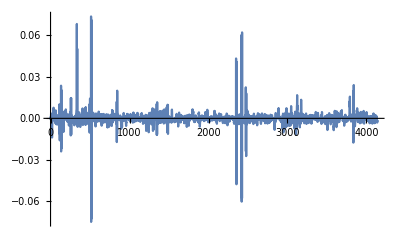

```mathematica
ListLinePlot[rsWethUsdc90dFilteredLastMo, PlotRange->All]
```

```mathematica
edistWethUsdc90dFilteredLastMo = EstimatedDistribution[rsWethUsdc90dFilteredLastMo, StableDistribution[1, aWU90dLM, bWU90dLM, locWU90dLM, scaleWE90dLM]]
```

StableDistribution[1,1.58793,-0.0706768,-0.000101131,0.00135632]

```mathematica
edistWethDai
```

StableDistribution[1,1.60712,-0.108702,-0.000176324,0.00134358]

```mathematica
(* It's not terrible in terms of alpha difference but likely manifests in extreme fashion for inverse CDF? *)
```

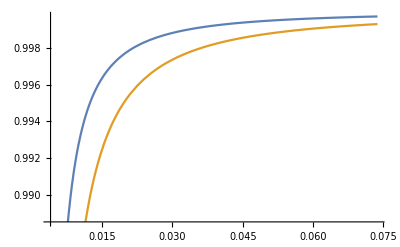

```mathematica
Plot[{CDF[edistWethUsdc90dFilteredLastMo,x],CDF[edistWethUsdc90dFiltered,x]},{x,0.004,Max[rsWethUsdc90dFiltered]}]
```

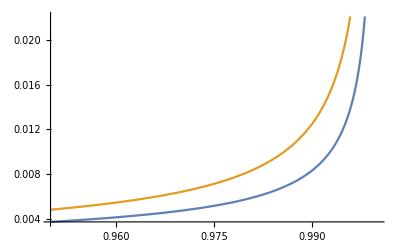

```mathematica
Plot[{InverseCDF[edistWethUsdc90dFilteredLastMo,x],InverseCDF[edistWethUsdc90dFiltered,x]},{x,0.95,1.0}]
```

```mathematica
InverseCDF[edistWethUsdc90dFiltered,0.99]
```

0.0124991

```mathematica
InverseCDF[edistWethUsdc90dFilteredLastMo,0.99]
```

0.00831473

```mathematica
InverseCDF[edistWethUsdc90dFiltered,0.99] / InverseCDF[edistWethUsdc90dFilteredLastMo,0.99]
```

1.50325

```mathematica
(* Factor of 1.5 difference ... Not terrible especially if we're conservative with k values: k ~ e**(F^{-1}(1-alpha)) *)
```

```mathematica
Exp[InverseCDF[edistWethUsdc90dFiltered,0.99]]
```

1.01258

```mathematica
Exp[InverseCDF[edistWethUsdc90dFilteredLastMo,0.99]]
```

1.00835

```mathematica
(Exp[InverseCDF[edistWethUsdc90dFiltered,0.99]] - Exp[InverseCDF[edistWethUsdc90dFilteredLastMo,0.99]])/Exp[InverseCDF[edistWethUsdc90dFilteredLastMo,0.99]]
```

0.00419318

```mathematica
(* 0.4% difference in value we care about ... Yea not massive *)
```

```mathematica
(* Compared with normal dist fit? *)
```

```mathematica
eNormdistWethUsdc90dFiltered = EstimatedDistribution[rsWethUsdc90dFiltered, NormalDistribution[uWethUsdc, sWethUsdc]]
```

NormalDistribution[-5.27153×10^-6,0.00489882]

```mathematica
InverseCDF[eNormdistWethUsdc90dFiltered, 0.99]
```

0.0113911

```mathematica
(* Interesting, close ... *)
```

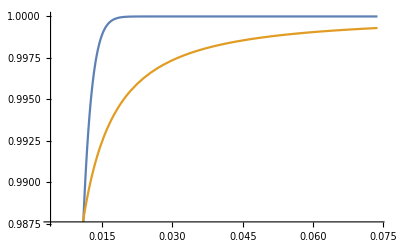

```mathematica
Plot[{CDF[eNormdistWethUsdc90dFiltered,x],CDF[edistWethUsdc90dFiltered,x]},{x,0.004,Max[rsWethUsdc90dFiltered]}]
```

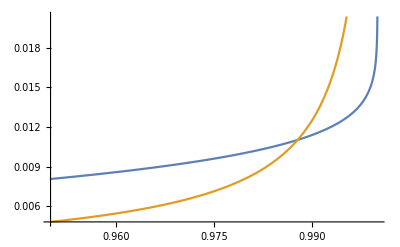

```mathematica
Plot[{InverseCDF[eNormdistWethUsdc90dFiltered,x],InverseCDF[edistWethUsdc90dFiltered,x]},{x,0.95,1.0}]
```

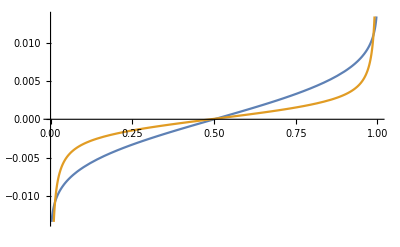

```mathematica
Plot[{InverseCDF[eNormdistWethUsdc90dFiltered,x],InverseCDF[edistWethUsdc90dFiltered,x]},{x,0,1.0}]
```

```mathematica
(* More around 0.999 mark where divergence is bad. Less so for stable v. stable w diff alpha *)
```

```mathematica
InverseCDF[edistWethUsdc90dFiltered,0.999]
```

0.0576731

```mathematica
InverseCDF[edistWethUsdc90dFilteredLastMo,0.999]
```

0.0332197

```mathematica
InverseCDF[eNormdistWethUsdc90dFiltered,0.999]
```

0.0151332

```mathematica
(* yes, much bigger difference here ... and even worse at 0.9999 *)
```

```mathematica
InverseCDF[edistWethUsdc90dFiltered,0.9999]
```

0.276565

```mathematica
InverseCDF[edistWethUsdc90dFilteredLastMo,0.9999]
```

0.140854

```mathematica
InverseCDF[eNormdistWethUsdc90dFiltered,0.9999]
```

0.0182135

```mathematica
(* Still remains about a factor of 2 between stable v stable w differing alphas. HOWEVER, becomes factor of 10 at 99.99% confidence bw normal and stable *)
```

```mathematica
Exp[InverseCDF[eNormdistWethUsdc90dFiltered,0.9999]]
```

1.01838

```mathematica
Exp[InverseCDF[edistWethUsdc90dFilteredLastMo,0.9999]]
```

1.15126

```mathematica
Exp[InverseCDF[edistWethUsdc90dFiltered,0.9999]]
```

1.31859

```mathematica
(* which in VaR calc of Exp[F^{-1}] - 1 translates to k jumping from 0.018 up to 0.15 / 0.32 .... *)
```

```mathematica
(* So yes we likely want more data and use stable. Report fits on both rolling 30d basis and full set of data (or longer time frame). *)
```

```mathematica
(* Compare first month w last month of ETH/USDC *)
```

```mathematica
rsWethUsdc90dFilteredFirstMo = Table[rsWethUsdc90dFiltered[[i]], {i, 1, 5000}]
```

{-0.00120673,0.000176452,-0.0000603568,-0.000373722,-0.000389599,0.000559858,-0.00092094,-0.00154871,-0.000905547,-0.000584311,-0.00172231,-0.00371162,-0.00218903,-0.00259613,-0.00374997,-0.00385087,-0.00499694,-0.00681335,-0.00674886,-0.00538641,-0.00238816,0.0014468,0.00178939,0.000805576,-0.0000377299,-0.00155115,-0.00338662,-0.00382918,-0.00321668,-0.00270154,-0.00132964,0.000186854,0.00248069,0.00193942,0.00361139,0.00131712,0.00210643,0.00262488,0.00257794,0.00174097,0.00254967,0.00294714,0.00224079,0.00201131,0.00100575,-0.00125599,-0.00167678,-0.00119665,-0.00236811,-0.00157824,-0.00332412,-0.00354818,-0.00450461,-0.00398038,-0.00322619,-0.00304323,0.000142204,0.000979734,0.0021921,0.00450208,0.00447003,0.00571894,0.00373655,0.00548546,0.00235632,0.00100711,0.00263737,0.000611337,-0.000136787,3.23868×10^-6,0.000777499,0.00199232,0.00303221,0.00327366,0.0033268,0.00307257,0.00216783,0.000783838,-0.000080765,0.000712625,0.000341638,-0.00024731,-0.00129321,-0.000717748,-0.0014396,-0.000834414,0.0000370664,0.000883407,0.00188126,0.00330856,0.0033331,0.00375294,0.00315136,0.000968898,-0.000801161,-0.00274671,-0.00394275,-0.00478984,-0.00467682,-0.00443888,-0.00235901,-0.000880246,0.00120961,0.00528268,0.00433957,0.00635964,0.00568107,0.00541609,0.00487764,0.00308507,0.00410442,0.00120017,0.00197393,0.00275295,0.00157799,0.00366619,0.00206488,0.00133458,0.000382621,-0.0000699762,0.00016049,0.00183379,0.00206868,0.00300834,0.00278611,0.00253281,0.00150304,0.0000776621,-0.000766576,-0.000219429,0.00062098,0.000245869,0.00224434,0.00260876,0.00210895,0.000646611,0.00125299,-4.26556×10^-6,-0.00153047,-0.00196873,-0.000776981,-0.000962884,0.00028361,0.0000302359,0.000690131,0.0000496851,0.00153279,0.00162621,0.00174437,0.000266823,-0.0012285,-0.00483641,-0.00409798,-0.00398706,-0.00134311,0.000485584,0.00229321,0.00220958,0.000161885,-0.0000742672,0.000928476,0.000205861,0.00101243,0.000866467,0.000885114,-0.000199799,-0.00127449,-0.00280245,-0.0033278,-0.00277031,-0.000607151,-0.00189991,0.000708547,0.000977043,0.00122085,0.000341527,0.000403759,-0.000586693,-0.000678702,-0.000395253,0.000632638,0.000902484,0.00103304,0.00270694,0.00160654,-0.000847635,-0.00119222,-0.00175055,-0.00249942,-0.00194127,-0.00137353,-0.0013237,-0.000759113,-0.000822173,-0.000615807,0.00114548,0.00105966,0.000674579,0.00162314,0.00101654,0.000823438,0.00060543,-0.000267887,-0.000910003,-0.00234046,-0.00258329,-0.00313232,-0.00231122,-0.00201389,-0.0022762,-0.00161991,-0.00147791,-0.0000243955,0.00067665,0.0060331,0.00668285,0.00927214,0.00797051,0.00902686,0.00389741,0.00219452,0.00210222,0.000445539,0.00103525,0.00128522,0.000247569,0.0011596,0.00361498,0.00495561,0.00529279,0.00420697,0.00408244,0.000438949,-0.000374359,-0.000597394,0.00204706,0.00254348,0.00195034,0.0000247282,-0.000905713,-0.00238829,-0.00181462,-0.000955324,-0.00165848,-0.00166356,-0.000448398,-0.0000418368,-0.000962198,-0.000526023,-0.000771889,-0.00113149,-0.00087899,0.000785294,0.00210836,0.00254428,0.00193499,0.000597359,-0.000959418,-0.00173637,-0.00221478,-0.0032536,-0.00200872,-0.00166366,-0.00528351,0.00228401,-0.000396164,-0.00140414,-0.00116982,0.00374935,-0.00420261,-0.00273237,-0.00157084,-0.00223279,-0.00405097,-0.00261365,0.000508622,0.00103635,-0.000164515,-0.0000628882,-0.000951101,-0.000162466,0.000665113,0.00251147,0.00592911,0.00806295,0.00596692,0.00549004,0.00330576,-0.000737829,-0.00550944,-0.00680145,-0.00387939,-0.00231952,0.000446972,0.00514113,0.0043007,0.00136402,-0.00100532,-0.00136694,-0.00138374,-0.00102386,0.000420436,0.00251006,0.00290296,0.00302551,0.00287687,0.00101647,0.00130164,0.0009427,0.00163272,0.00355894,0.00254027,0.00534872,0.00328251,0.000504665,-0.000189969,-0.000860302,-0.00234141,-0.00133308,-0.000212404,-0.000577845,-0.000651895,-0.000569861,-0.00188448,-0.00219684,-0.00299699,-0.00218893,-0.00093305,0.00102137,0.00148281,0.00397436,0.00296892,0.00417452,0.00277819,0.0021355,0.00139401,0.00222117,0.00218928,0.00276008,0.00360778,0.00444973,0.00416209,0.00330268,0.00318243,0.0027957,0.00224798,0.00145072,0.00158945,0.000651551,-0.00122243,-0.00100825,-0.0001823,0.0000705225,-0.000749663,-0.000746842,0.000326147,-0.000404649,0.00054826,0.00273891,0.00300199,0.00219743,0.00106368,0.000615812,-0.000113195,0.000718815,0.0022022,0.00261939,0.0036032,0.00383303,-0.000961861,-0.00216249,-0.00328255,-0.00409711,-0.0126016,-0.00504819,-0.00349995,-0.000706687,0.00103729,0.00136636,-0.00120346,-0.00338883,-0.00431124,-0.00296884,-0.00108496,0.0000695733,0.00142483,-0.0023581,-0.00553602,-0.00727636,-0.0092007,-0.0118317,-0.0107324,-0.00400684,-0.00258077,-0.000348289,0.00414171,0.00622641,0.00211121,0.000154442,0.000745415,-0.000588753,-0.00172617,-0.000141715,0.00208687,0.00152084,0.0015393,-0.000833912,-0.00201515,-0.00103073,0.000283345,-0.00115785,-0.00157559,-0.00214027,-0.00500302,-0.00799012,-0.00601438,-0.00694454,-0.00459589,-0.00846632,-0.0138003,-0.0127245,-0.00823448,-0.00693386,3.57542×10^-6,-0.00603135,0.0156081,0.00445268,0.0027864,0.00281029,0.0101999,-0.0114221,-0.000911608,-0.00357121,-0.0062516,-0.00219527,-0.00662301,-0.00450093,-0.000491038,0.00115676,0.000382632,0.00306648,-0.00141802,-0.00508591,-0.0033121,-0.00198609,0.000196775,0.00318695,0.00105543,-0.00314687,-0.00493772,-0.0062809,-0.00669001,-0.00197024,0.002545,0.00397548,0.00664627,0.00506877,0.00290276,0.000112059,0.000552199,-0.000258701,0.00278543,0.00554231,0.00672165,0.00870246,0.0058659,0.00278655,0.00256674,0.00239826,0.00237098,0.00120443,0.00266766,-0.000104853,-0.00174875,-0.00361806,-0.00177669,-0.00377022,-0.00261829,-0.00314037,-0.00395221,-0.00546506,-0.00215465,-0.00114284,0.00177262,0.00463417,0.00691103,0.00487133,0.00370479,0.00227567,-0.000406678,0.000569698,0.00289343,0.00389197,0.00468766,0.00583437,0.00210819,0.00231993,0.000128694,-0.000935311,-0.00134891,-0.000956703,-0.00512835,-0.00246365,-0.000600981,-0.000159904,0.00141108,0.00515938,0.00353114,0.00427087,0.00242524,0.00106617,0.00053809,0.000319866,0.00174101,0.00169106,0.00115526,0.00099856,-0.00089797,-0.00263275,-0.00228707,-0.000550966,-0.00118163,-0.00124948,-0.000957185,-0.00252525,-0.00283688,-0.00256824,-0.00164856,0.000120219,0.00140416,0.00139857,0.00220359,0.00216545,0.00178297,0.0033324,0.00215588,-0.00109466,0.00139342,-0.00942686,-0.00789698,-0.00787459,-0.00469481,-0.00744448,0.00384828,0.000848758,0.000367058,-0.00213207,-0.00301034,-0.00183259,0.000645233,0.000492977,0.00390305,0.00656524,0.00370489,0.00413998,0.00228553,0.000542292,-0.00167351,-0.000141523,-0.000404621,0.000174401,0.000815721,0.00153486,-0.000492745,-0.000207424,-0.000332305,-0.0000290578,0.000860051,0.00107633,0.00105768,-0.000115579,-0.00192669,-0.00277235,-0.0024697,-0.00431359,-0.00412185,-0.00118579,-0.000975521,-0.000461467,0.000589419,0.00163457,0.00169184,0.0014601,0.00180705,-0.000527823,-0.00163603,-0.00307266,-0.00280879,-0.00282746,-0.00119031,-0.00259338,-0.00269458,-0.00441814,-0.00421308,-0.00487301,-0.00384606,-0.0024068,-0.00116728,-0.00062649,-0.00235755,-0.001129,0.00020115,-0.000197578,-0.000657545,0.00420281,0.00501052,0.00178519,0.00206233,0.00162655,-0.000448803,-0.00122814,-0.000879599,-0.00228374,-0.00145558,-0.00227247,-0.000861159,-0.000950716,-0.00165397,-0.000283907,0.00123609,0.00278327,0.00346455,0.00732741,0.00421292,0.0022428,0.00119173,-0.000244369,-0.000938577,-0.000866448,-0.00315846,-0.00195881,-0.000822664,0.000449665,0.00176114,0.00654132,0.00442676,0.00273136,0.00219691,0.00225034,-0.000494392,-0.000455288,0.0000653734,0.000162442,-0.000293995,-0.00113959,-0.000445806,0.000559219,0.00113625,0.00165103,0.0023337,0.00167441,0.00038733,-0.000264483,-0.00014555,-0.000721203,-0.0013545,-0.00131775,-0.00148765,-0.00368341,-0.00255773,-0.00183317,-0.00110648,-0.00184839,-0.00357169,-0.00268691,-0.00135763,-0.00118826,-0.00259678,-0.000441151,-0.000689152,-0.00106823,-0.00101267,0.00155722,0.00191746,0.0023195,0.00228884,0.00135436,0.000287349,0.000402753,0.000133519,0.000359978,0.000207549,-0.000834001,-0.00217155,-0.00214295,-0.00421486,-0.00481491,-0.00414322,-0.00272072,-0.00224655,-0.00133937,-0.000807712,0.0002067,0.000593348,0.000970919,0.00145467,0.00165921,0.000482959,0.000376061,0.000136985,-0.000109334,-0.000126934,-0.000581944,-0.000879138,-0.00206599,-0.0018632,-0.00180305,-0.000997964,0.000552587,0.000589507,0.00114622,0.00215245,0.00119253,0.0027759,0.00384843,0.00323833,0.00188691,0.000715281,-0.00139645,0.00138431,0.0028638,0.00487441,0.00650475,0.00572486,0.00190231,0.000508831,-0.00163774,-0.00105941,0.000355478,0.000561101,0.0017383,0.00239054,0.00275324,0.00379113,0.00269575,0.00209498,0.00234747,0.000789187,0.000888326,0.00106607,0.0000390036,-0.0000525149,-0.0000821205,-0.000556964,0.000461147,0.00167898,0.00102753,0.00253293,0.00325176,0.00215814,0.00165608,0.000163246,0.000269869,0.000040018,-0.00118776,-0.000608973,0.000444086,0.000266682,0.0000139491,0.00115176,-0.000157003,-0.0018536,-0.00156399,-0.00143625,-0.00181795,-0.00172224,-0.000951319,-0.0027338,-0.00290476,-0.00252172,-0.00194732,-0.0004145,-0.000291751,0.000606317,-0.000385714,-0.00267611,-0.0025355,-0.00115107,-0.00132192,-0.00200004,-0.00457616,-0.00559553,-0.00429184,-0.00661355,-0.00646869,-0.00155098,0.000668081,0.000853597,0.00374922,0.00604024,0.00552838,0.00478614,0.00206674,0.00275674,0.00438478,0.00272398,0.00193095,0.00311733,0.00756794,0.00913441,0.00897017,0.00804286,0.0077439,0.00482622,0.00199162,0.00162826,0.00249967,0.00292999,0.00318709,0.00334572,0.000962092,-0.000387674,-0.000873219,-0.000166592,-0.000589148,0.00165579,0.00136832,0.000670425,-0.0000450499,0.000227281,0.00097717,0.00165013,0.00142033,0.000842973,0.000234833,-0.000560104,-0.00218888,-0.00153094,-0.000487778,0.0000201364,0.000171513,0.00236449,0.00259948,0.00211419,0.00243991,0.00193531,-0.000109346,-0.00162508,-0.00240107,-0.00241968,-0.00186829,-0.00116043,-0.000866059,-0.00110812,-0.0011947,-0.00158624,-0.00124399,-0.000265758,-0.000294621,-0.00092884,-0.000592053,0.00221002,0.00327831,0.00304925,0.00529694,0.00459602,0.00108425,0.000509407,0.00060931,0.00127141,0.0015676,0.00223282,0.00302034,0.00244967,0.000842439,-0.000652185,-0.000480236,-0.000902864,-0.00203126,-0.00120842,-0.00174557,-0.00179562,-0.000365795,0.000516376,0.000600133,0.000788552,-0.0000507764,-0.00205586,-0.000868774,-0.000639892,-0.000710718,-0.0000478221,0.000538015,0.000799382,0.00141177,0.000242582,-0.000230628,-0.00222298,-0.0016392,-0.00211303,0.00115072,0.00293122,0.00471373,0.00239054,0.00279118,0.000304917,-0.000603432,-0.00208368,-0.00169736,-0.00124682,-0.0012971,-0.000776473,-0.00064134,-0.000571684,-0.000610072,-0.000415267,-0.000689104,-0.0010389,-0.00104936,-0.00114247,-0.00389013,-0.00287061,-0.00345415,-0.00146925,0.000809617,0.00315623,0.00449341,0.0077896,0.00491217,0.00285559,0.00159224,0.00154276,-0.000965606,-0.000133131,-0.0000589046,0.000575507,0.00130704,0.00118483,-0.000446293,-0.000308394,-0.00101341,-0.00121398,-0.00184522,-0.000121873,-0.0000669166,0.000202302,0.000011791,0.0000613097,0.000877181,0.00092317,0.000681095,0.00102483,0.000978949,0.000449505,-0.000546981,-0.00178726,-0.0019691,-0.00237213,-0.00218041,-0.00175071,-0.000352776,0.000179633,0.000135227,0.000288145,0.000817332,0.00144868,0.0020547,0.00232534,0.00244505,0.00120557,0.00133906,0.00287408,0.00157919,0.00204595,0.00179106,0.00192126,0.000724835,0.000382512,0.000375168,-0.000228686,-0.000503744,-0.000898399,-0.000763558,-0.000607949,-0.000116725,-0.000199824,0.0000961991,-0.000569861,-0.000306774,-0.000210067,0.000307569,0.000141434,0.000924759,0.000448156,-0.000084335,-0.000202221,-0.00025325,-0.000526525,-0.000136104,0.000788527,0.000945125,0.00114049,0.00157497,0.00167556,0.00135261,0.00159875,0.000749986,0.0000842274,-0.000902854,-0.00104242,-0.00116856,-0.000918878,-0.000989948,-0.000842766,-0.0010209,-0.00102635,0.000980125,0.00466948,0.00435123,0.00699025,0.00655278,0.00483603,0.00138255,0.00181332,0.00206437,0.00261004,0.00139139,0.0026052,0.000192994,-0.000594479,-0.00191702,-0.000874915,-0.00177684,-0.00119709,-0.00118025,0.0000498224,-0.0000695999,-0.000173381,-0.000463836,0.000109768,0.000148284,-0.000310118,0.000274326,0.000552073,-0.00118885,-0.00203713,-0.00186567,-0.000657554,-0.000552606,0.000677591,0.00176288,0.00167314,0.000343884,0.000628297,0.000467979,-0.000348427,0.0006145,0.00054536,-0.000128062,-0.000416618,-0.000521026,-0.0015129,-0.00191137,-0.000968557,0.0000143828,0.00106242,0.00156105,0.00297838,0.00404862,0.00454336,0.00323331,0.00278779,0.00188643,0.00074969,0.000215854,0.000703627,0.00120311,0.0015477,0.00117297,0.00119751,-0.0000595017,-0.00130719,-0.00275445,-0.00369014,-0.00390995,-0.00416706,-0.00331629,-0.00267624,-0.00124081,-0.000435451,0.00023022,0.000462324,0.000644081,-0.000343244,-0.000732279,-0.000314967,-0.000838453,-0.0024047,-0.000602897,-0.00200062,-0.00429456,-0.00314678,-0.00368357,-0.000863389,-0.00298032,0.000781605,0.00146051,0.00267362,0.00156457,0.00253169,0.00152362,0.00112573,0.000719234,0.000428393,0.000405166,-0.000222705,-0.0015047,-0.00186106,-0.002133,-0.00157837,0.0000362676,0.000672393,0.00185016,0.00217979,0.00179423,0.0016508,0.00283524,0.00313298,0.00340067,0.00455065,0.00579742,0.00377328,0.00360246,0.00312079,0.00222869,0.00140936,0.000989776,0.00169525,-0.00242705,-0.00209561,-0.0018528,-0.00209557,-0.000946723,0.00186983,0.00171426,0.00196074,0.00149224,0.00033871,-0.00115616,-0.00189843,-0.00357131,-0.00211127,-0.00228,-0.000137593,0.000618353,0.00150091,0.00170323,0.00267142,0.00171991,0.00190605,0.00151379,0.00109552,0.000747929,-8.32535×10^-6,-0.0000696488,0.00123753,0.00114301,0.000810575,-0.0414512,0.0419846,-0.000682734,-0.0011462,-0.0000871902,0.041082,-0.0388866,-0.0086889,0.00695421,-0.000777239,-0.00195428,-0.00185956,0.00843883,-0.0090184,-0.0000178437,0.0012989,0.00316076,0.00380601,0.00280303,0.000709552,-0.000329469,-0.00221543,-0.00344843,-0.00155582,-0.000329168,-0.0000441934,0.000735073,0.00259507,0.00167799,0.00139987,0.00114346,0.00037167,-0.000835275,-0.00126008,-0.00214914,-0.00193602,-0.00151427,-0.00155432,-0.000963495,0.000344132,0.000623351,0.000445749,0.000462623,0.0000709405,-0.000302673,-0.000857178,-0.000336417,-0.000315789,-0.000821418,-0.00233291,-0.00191269,-0.0022671,-0.00199191,-0.000830382,-0.000560195,-0.0000881161,0.000826126,0.00100014,0.000773918,0.0017694,0.00187312,0.0014366,0.00149527,0.00126627,0.00209366,0.00110499,0.00131611,0.000622154,0.00024545,0.000265324,0.000329664,-0.000106138,-0.000108165,-0.00056995,-0.00112594,-0.000854892,-0.00109436,-0.00102154,0.00100342,0.00273074,0.00301677,0.0037619,0.00375775,0.00245633,0.000342655,0.000150083,-0.000116608,-0.000196338,0.000114894,0.000638325,0.000272947,0.0000955498,0.000132804,-0.000321559,-0.000631006,0.000643513,0.0013194,0.00149388,0.00202969,0.0021509,0.000318524,-0.00045603,-0.00101728,-0.00158425,-0.00245614,-0.00157256,-0.00106742,-0.000512263,0.000120067,0.000483341,0.000529602,0.000982815,0.00175016,0.00120714,0.00128144,0.00122909,-0.000382203,-0.00189347,-0.002069,-0.00248612,-0.00286884,-0.00371627,-0.00223168,-0.00119364,-0.00124053,0.00021558,-0.000951067,-0.00183928,-0.00191845,-0.00145192,-0.00188646,0.00106149,0.00129213,0.00103251,0.000932346,0.000880728,-0.0000126498,-0.0016209,-0.00262868,-0.00101439,-0.000917749,-0.00153729,0.0000288463,0.00102805,0.0000462368,-0.000223226,0.00117025,0.00220649,0.0026161,0.0029575,0.00270385,0.00283155,0.0017771,0.00154787,0.000945675,0.000489633,0.000191487,-0.0000167517,-0.00015439,-0.000620863,-0.00180333,-0.000406361,-0.00101402,-0.00116203,-0.00121671,-0.000429419,-0.00150654,-0.000298645,0.000396086,0.00096187,0.000640243,0.000714087,-0.000611885,-0.000655001,-0.000031475,-0.000359274,-0.000301282,0.000208999,0.00048424,-0.000402084,0.000406336,0.000705886,0.00111772,0.00102443,0.00121048,0.0012271,0.000721953,0.000623852,0.000554546,0.000440623,0.000299463,0.000211864,0.000377373,0.000588372,0.0011471,0.00120216,0.00130684,0.00136994,0.00061367,-0.0000851429,-0.0000897249,-0.000529571,-0.000431752,-0.000831333,-0.000470113,-0.000540893,-0.000233389,0.000474922,0.00121517,0.0012423,0.00687042,-0.00439132,-0.00022816,-0.000427838,0.0145414,-0.0214728,0.00490606,-0.000106052,-0.00109714,-0.0178032,0.0139376,-0.001578,-0.00204077,-0.00145424,-0.000911688,-0.000986064,-0.000957783,-0.00063972,0.000279193,0.000616705,0.000661391,-0.000181405,-0.000182426,-0.000452632,-0.000701488,-0.00100204,0.000828089,0.000936799,0.00119491,0.00142162,0.000730048,-0.0010337,-0.00064549,-0.000901503,-0.000834874,-0.0000124756,-0.000112099,0.0000744141,0.000335802,0.000209805,0.000403169,0.00145046,0.00136271,0.00110441,0.000845306,0.000787364,-0.0000138236,0.000380087,-0.0000181431,9.66408×10^-6,0.000179784,-0.0000714102,-0.000309686,0.000421643,0.00117555,0.00122649,0.00100583,0.000777633,0.000476592,-0.0000828325,-0.000651464,-0.000751128,-0.000666225,-0.000875066,-0.000950376,-0.000825752,-0.00130323,-0.000730362,-0.000554217,-0.000474488,-0.000175335,0.000199862,-0.00040209,-0.000365556,-0.00054007,-0.0000890267,-0.000144091,0.000480641,0.000898759,0.00121699,0.0013267,0.00146877,0.000785515,0.000415181,0.000110056,-0.0000248417,-0.000334675,-0.000252165,-0.000479,-0.0000305659,0.000414973,0.00384283,0.00464208,0.00459038,0.00368655,0.00497468,0.000773252,1.38813×10^-6,-0.000248345,0.000728654,0.000632891,0.000806726,0.00112336,0.000978499,0.000167927,-0.0000516025,-0.000132285,-0.000172418,-0.0000546051,0.00107165,0.00164232,0.00173899,0.00117991,0.00128991,-0.000548989,-0.000770046,-0.00104571,-0.000414962,0.00026135,0.000389526,0.000108301,0.0000929041,-0.000114462,-0.000323705,-0.000126862,0.000330517,0.000496064,0.000213113,-0.000167446,-0.00139237,-0.00272959,-0.00232198,-0.00172782,-0.000684152,0.000231279,0.000995399,0.00050165,-0.000188684,-0.000769504,-0.0000244679,0.00099389,0.00124882,0.00156672,0.00141812,0.00113295,0.000454937,0.000420587,0.00130814,0.00155827,0.00131251,0.00135534,0.000837613,0.000137285,-0.000387778,-0.000451854,-0.000511923,-0.000313462,-0.00010025,-0.0000708208,-0.000263446,-0.000140434,-0.000482702,-0.000815066,-0.00112947,-0.000797436,-0.00134519,-0.000575632,0.000204589,0.00166638,0.0016478,0.00242032,0.00200975,-0.024293,0.0287025,0.00241599,0.00262571,0.00247084,0.0287808,-0.024599,0.00101865,0.00101533,0.000728176,0.000305472,0.000195423,0.000356933,0.000212255,-2.8602×10^-7,-0.000239674,-0.00103511,-0.00132637,-0.000243642,-0.000486028,0.000372106,0.00153891,0.0017067,0.00118684,0.0325148,-0.0323952,-0.00123801,-0.00107113,-0.000947338,-0.0272633,0.0274025,0.000942134,0.000724385,0.000939389,0.000352002,0.000550232,0.000914905,0.000628839,0.000935858,-0.00011343,-0.000281164,-0.000675134,-0.000591396,-0.000761658,-0.000398219,-0.000572141,-0.000255126,-0.0000255528,0.0000943235,0.00038541,0.000760633,0.00123961,0.000831282,0.000754185,0.000779138,0.000484623,0.0000428802,-0.000424447,-0.00208702,-0.00246332,-0.0039297,-0.00428938,-0.000577303,0.000242626,0.0000245399,0.000825934,0.00105264,-0.0000251619,-0.000716084,0.000179684,0.000199738,0.000297906,0.000168538,0.000115773,-0.000192196,-0.000645087,-0.00193845,-0.00193054,-0.00152017,-0.00167191,-0.00107768,-0.00121486,-0.00119745,-0.00173691,-0.00161948,-0.000748798,0.000209102,0.000428268,0.000734845,0.000650775,0.00106822,0.00124182,0.00227413,0.00236237,0.00269409,0.00165144,0.00127944,0.000140168,-0.000212721,-0.000154803,-0.0000187387,0.00024798,0.000754791,0.00119451,0.00112729,0.000954665,0.000378853,-0.000311067,-0.000222788,-0.000307194,0.0000524551,-0.00049898,-0.000822251,-0.000462705,-0.000779924,-0.000648556,0.0000669315,0.000405771,0.000312875,0.000132004,-0.0000905182,-0.0359786,0.0363046,0.000719188,0.000887844,0.00099192,0.0392383,-0.0373389,0.000206924,0.000342924,0.000147036,-0.0000812063,-0.0000587938,-0.000010622,0.0000676669,0.000470984,0.000573227,0.000683607,0.000486529,0.00116536,0.00137443,0.00126916,0.00221239,0.00210869,0.00136684,0.00111328,0.000556192,4.68688×10^-6,-0.000322991,-0.000525033,-0.000536487,-0.000511655,-0.000431705,0.000109535,0.000572768,0.000679499,0.000717861,0.0000733799,-0.0012067,-0.00178257,-0.00263177,-0.00309087,-0.00156029,-0.000561773,0.000348814,0.000448087,0.000741062,0.00179748,0.00209749,0.00311744,0.00242346,0.00295951,0.00106534,0.000726196,0.000531729,0.000642593,0.00207244,0.00198173,0.00145474,0.00181094,0.00119526,-0.0000490975,0.000415406,0.000611772,0.0014115,0.00154647,0.00167922,0.00156765,0.00175257,0.00165708,0.00100607,0.000475822,0.000133392,-0.000329116,-0.000433984,0.000604679,0.000488353,0.00172646,0.00300421,0.00327459,0.00199304,0.00110795,0.000996769,0.000117901,-0.000265054,-0.00057575,-0.000449893,0.000990467,0.0032076,0.00328159,0.00294208,0.00378181,0.00268727,0.00198293,0.00258181,0.00321178,0.00243213,0.00144033,-0.00101848,-0.00100298,-0.00112721,-0.000910306,0.000869275,-0.000377356,-0.00103542,-0.00152943,-0.001569,-0.00207574,-0.000185879,0.000708944,0.00165033,0.00164907,0.00174654,0.000590943,0.0000731581,-0.000917137,-0.00171684,-0.0026487,-0.00158419,-0.000924789,-0.00157356,-0.000800716,-0.000225496,-0.00233173,-0.00216651,-0.00138314,0.000223727,0.000821374,0.00270273,0.00422558,0.0033642,0.00176459,0.0024482,0.00168429,-0.0000629361,0.0000132796,0.00049209,-0.000300669,-0.000369268,0.00319694,0.00566947,0.00476461,0.00604239,0.00532524,0.00430516,0.0013428,0.00152603,0.00288647,0.00176983,0.00150136,0.00240793,0.00248646,0.00171193,-0.0000785452,-0.00165977,-0.000715552,-0.00111037,-0.00223867,-0.00109765,0.000818495,-0.00133836,-0.00203,-0.00011995,-0.0000860915,-0.000128324,0.0000563381,0.00117238,-0.000158133,0.00174783,0.00287387,0.00584965,0.00576358,0.00558716,0.00394461,0.00241308,0.0021106,0.00192353,0.00317306,0.00338297,0.00283384,0.0248727,-0.0295747,-0.00383283,-0.00312703,-0.00851689,-0.0327107,0.0239553,-0.00499594,-0.00491803,0.000593634,0.000786451,-0.00052929,-0.00289306,-0.0028111,-0.00220873,-0.00387005,-0.00423728,-0.000974656,-0.00045358,-0.00038493,0.00121984,0.000662481,0.000182991,0.00262872,0.00301494,0.00350616,0.00492893,0.00553839,0.00516567,0.00351876,0.00380111,0.00157244,0.00209146,0.00120385,0.000637409,0.000924354,0.00113682,-0.00025714,-0.00181377,-0.000730396,-0.000974799,-0.0012416,-0.00135503,-0.00119148,-0.00260131,-0.0040644,-0.00282087,-0.00174289,-0.00176069,-0.0014499,0.00222433,0.00218297,0.00380129,0.00368075,0.00269203,0.000260497,0.00085787,0.00160457,0.00182732,0.00401232,0.00475679,0.0026052,0.00121174,0.00205306,0.00300466,0.00256725,0.00305798,0.00237677,-0.0000541018,-0.00173103,0.000212214,-0.000311547,0.0023477,0.00313266,0.0144512,-0.00821527,-0.000233259,0.00056875,-0.0024141,-0.0136794,0.000907223,-0.00482629,-0.00769023,-0.00747064,-0.0072335,-0.00919936,-0.00783773,-0.00282945,-0.000552179,-0.0033097,-0.00492109,0.00136816,0.00209213,0.000817307,0.00210796,0.00522972,0.00402665,0.00189449,0.00252173,0.00251411,0.00316717,0.00382487,0.00245615,0.00212261,0.0024164,0.00348178,-0.0012568,0.00252062,0.00374274,-0.000014624,-0.0039969,0.00190518,-0.00181569,-0.00222069,0.000102459,-0.000351699,-0.00275528,-0.00307612,-0.0030861,-0.00445619,-0.00588402,-0.00278822,-0.00537252,-0.00111003,0.00106573,0.00149643,0.00119183,-0.00123869,-0.00321451,-0.00172741,-0.000772273,0.000197519,0.00399308,0.00389842,0.00285734,0.00352615,0.00349761,0.00249881,0.00279715,0.00276691,-0.000309147,-0.0000601254,-0.00173293,-0.00264434,-0.00202092,-0.00361974,-0.00439218,-0.00228394,-0.00179277,-0.00031246,-0.00038357,0.000503898,0.000934868,-0.000200978,-0.00243319,-0.00339921,-0.0025272,-0.00178304,0.0001005,0.000836132,0.000904455,0.0000406236,-0.00189845,-0.00266516,-0.00164924,-0.000771383,0.000356698,0.00163991,0.00280642,0.0033015,0.00506714,0.00617555,0.00352987,0.00374607,0.00350605,0.00078303,0.000772759,-0.000500961,-0.000762605,-0.000359629,0.000727157,0.00293034,0.00263243,0.00132018,0.000951084,-0.000238197,-0.00100745,-0.00100096,-0.000407248,-0.000553453,-0.000566249,-0.00122448,-0.000856886,0.000767422,0.00107443,0.000781722,0.000444886,0.000863504,-0.0000132857,-0.0000705493,0.000532784,0.00019341,0.000572388,-0.00114746,-0.00275928,-0.00435216,-0.00310706,-0.00183402,-0.000973186,0.000272731,0.00229309,0.000305783,-0.00208151,-0.00127732,-0.00143341,0.00060919,0.00394767,0.00593063,0.00555928,0.00908481,0.00489599,0.000869042,0.000140593,-0.00129995,-0.00165116,-0.00130949,-0.000303588,0.000118218,0.000053444,0.000206294,0.000918342,0.0014481,0.00173472,0.00290892,0.00244765,0.00315486,0.00174062,0.000488073,-0.0000586091,-0.00072441,-0.000917125,-0.000931368,-0.000178295,-0.00044664,-0.00179015,-0.00106988,-0.0007553,0.00152118,0.00273696,0.00596415,0.00310268,0.00628376,0.00189893,0.00125276,0.0012417,0.000266079,0.000119,-0.000399568,-0.0026541,-0.00267646,-0.00294734,-0.00256812,-0.00296245,-0.000972359,-0.000784195,0.000433367,0.000449396,0.000833865,0.00141228,0.00145332,0.000960328,0.000277953,0.000356543,-0.000698253,-0.00125817,-0.0014724,-0.00142044,-0.00110298,0.000240717,0.00129456,0.00120847,0.000966442,0.000170251,-0.00159325,-0.00239753,-0.00292885,-0.00194492,-0.000483647,0.000182052,-0.0000638852,0.000100221,-0.00174082,-0.00210883,-0.002491,-0.00265718,-0.000560939,-0.00164701,0.000912033,0.00131577,0.00239785,0.00196796,0.000937242,0.00184442,0.000563325,-0.000281282,-0.0003534,0.0000597015,-0.0000772389,0.000292661,0.000948287,0.00142395,0.00225833,0.00222131,0.00188461,0.00242533,0.00105813,0.000187083,-0.0000600749,0.000975249,0.00113938,0.00180085,0.000946857,0.00114737,-0.000210155,-0.000959771,-0.00196903,-0.000861534,-0.00137392,-0.000989096,-0.000269792,-0.000205979,-0.00056322,-0.0000886163,0.000523963,0.000747396,0.00156284,0.002812,0.00403125,0.00420561,0.00305489,0.0026046,0.0026826,0.00216038,0.00138547,0.00037401,0.000164857,-0.000396506,-0.000152172,-0.000405843,0.00075872,0.00123945,-0.00119557,-0.00236066,-0.00348023,-0.00742075,-0.00638938,-0.00552759,-0.00632436,-0.00490086,0.000445711,0.00224257,0.00044313,0.000962127,0.00105827,0.000109169,-0.00176864,0.000528903,0.00105145,0.00179383,0.00188006,0.00225211,0.00346089,0.00214399,0.00182764,0.00121772,0.00178012,0.000750892,0.000115139,-0.00102114,-0.00105887,-0.00204081,-0.00130553,-0.00222239,0.000904083,0.00067629,0.000316059,0.0010496,0.00126945,-0.00173688,-0.0019298,-0.00140729,-0.00251237,-0.00263919,-0.00127105,-0.000808188,-0.00146364,-0.00240915,-0.00179925,-0.00134519,-0.00153975,-0.00251534,-0.000622866,-0.0000259539,0.00012354,-0.0015684,-0.00266209,-0.00160165,-0.00256147,-0.00241131,-0.000363001,0.00161748,0.00078649,0.00110791,0.000866885,0.00108138,0.000162328,0.0010794,0.00177136,0.001546,0.0014765,0.00160927,0.000947748,0.00126002,0.00149442,0.00133562,0.000758814,0.000371539,-0.00137651,-0.00275927,-0.00281483,-0.00161339,-0.00142326,0.000470589,0.00182062,0.00120511,0.000949182,0.00184013,0.000820049,0.000916946,0.00138055,0.0012242,0.000783834,0.000258211,-0.00020784,-0.000529016,-0.00145782,-0.00050066,-0.000242408,-0.000190726,-0.000272342,0.00870858,-0.00938654,0.000226467,0.00135186,0.00214189,-0.00558612,0.0123582,0.00198154,0.00187331,0.00122904,-0.0000327771,-0.00035231,-0.000111837,-0.000915632,-0.000997477,-0.000817405,0.000491048,0.00123543,0.00144688,0.00131865,0.00367408,0.00318396,0.00290532,0.00326777,0.00201464,-0.0000197004,-0.000629549,-0.000354688,-0.000946516,-0.0000744153,0.000214734,0.000136544,-0.00138458,-0.00130297,-0.0014537,-0.00235215,-0.00113789,-0.000956286,-0.000715695,0.000167683,-0.000073345,-0.000781932,-0.00012715,-0.000326733,-0.0000108687,0.0000767404,0.000173384,-0.000711396,-0.0012155,-0.00227612,-0.00243543,-0.00215559,-0.000922316,-0.000348188,-0.000290524,0.000726065,-0.000702798,-0.00244335,-0.00241417,-0.00233529,-0.00204962,-0.000221369,0.000695697,0.00200261,0.00207223,0.00156893,0.000963892,0.00233496,0.00198935,0.00191329,0.00198049,0.00314483,0.00156601,0.00176995,0.0018349,0.00123532,0.000750063,0.000336193,-0.000201788,-0.000216785,-0.000988652,-0.000419541,-0.000342167,-0.000324196,-0.00025111,-0.0000132486,0.000464382,0.00106447,0.00229792,0.00252569,0.00188461,0.00230348,0.000165081,-0.00134994,-0.00134233,-0.00138248,-0.00167441,-0.000700946,-0.000438212,-0.000686447,-0.000712215,-0.00105928,-0.00109578,-0.00115833,-0.000922738,-0.00034599,0.0000328899,0.000453181,0.000697285,0.000964933,0.00152266,0.00269632,0.00215501,0.00176827,0.00118732,0.000169883,-0.00119999,-0.00131288,-0.000686424,0.0000260782,0.00124491,0.000539515,0.000311995,-0.000187368,-0.000784801,-0.00207383,-0.000995677,-0.00101084,-0.0000379421,0.000276334,0.00033208,0.0000498205,-0.000153706,0.000251057,0.000246037,0.00104269,0.000825627,0.00198544,0.00221282,0.00370657,0.00465255,0.00441804,0.0044784,0.00335551,0.00204703,0.00128545,0.0236239,-0.0215814,0.000892626,0.000817945,-0.00117677,-0.0233726,0.0254088,0.00361556,0.0047141,0.00714728,0.00766327,0.00370497,0.00421835,0.00393937,0.00100869,0.0014745,0.00237419,0.0000646105,-0.00015627,0.00108099,0.000278548,-0.0000291993,0.00106556,0.0000903253,-0.000506416,-0.00157183,-0.0013831,-0.000763981,0.00140743,0.000602496,0.00276716,0.00138255,0.00232088,0.000682154,0.00162766,0.00225019,0.00188019,0.00392805,0.00338308,0.0030612,-0.000705611,-0.000385554,-0.0017754,-0.00319005,-0.00267427,0.000512272,-0.000435567,-0.000113828,0.00120623,0.0016704,-0.000715668,-0.00242049,-0.00183339,-0.00126282,-0.00125467,0.000407135,0.0015933,0.00175303,0.00124896,0.000403527,-0.000606446,-0.000661656,-0.000364083,-0.000254914,0.00174212,0.0036066,0.0017302,0.00451918,0.000997394,-0.000733089,-0.0042658,-0.00273139,-0.00420842,-0.00085423,-0.000557168,0.00314565,0.00322806,0.00250835,0.00243235,-0.000375633,0.00180796,-0.000103922,0.00100169,0.00191945,0.00331461,0.00134777,0.00182497,0.00126491,-0.000521047,-0.000546575,-0.000765188,-0.000416963,-0.000959378,-0.000196021,0.000311696,0.000011184,-0.000925916,-0.000788498,-0.00121187,-0.00161215,-0.00191696,-0.00235332,-0.00170838,-0.0013512,-0.00292752,-0.000866122,0.000148203,-0.0000527912,0.000488796,0.00241671,0.00195636,0.000391473,-0.000634509,-0.0030682,-0.00461453,-0.00562987,-0.00574786,-0.00395106,-0.00575187,-0.00301677,-0.00101727,-0.000216769,-0.000565215,0.00251556,0.00259675,0.00240703,0.00119602,0.00255558,0.000341218,0.000856417,0.000939393,0.000994681,0.00108959,0.000631373,0.000108611,0.00310639,0.00578177,0.00463369,0.00452327,0.00256766,0.00471106,-0.00114186,-0.00191168,-0.000611302,-0.00100102,-0.00146098,-0.000238634,0.000842705,-0.000315055,-0.00031333,-0.000282625,-0.000738144,-0.00131135,-0.00100081,-0.00208771,-0.00134235,-0.00202946,-0.00121401,-0.000803067,0.000452666,0.000740171,0.00247809,0.00265119,0.00144515,0.00184186,0.00125848,0.000535616,-0.00035696,-0.000717763,-0.0000610798,-0.000417636,-0.000681036,-0.000797218,-0.00117583,-0.000650891,-0.00085598,-0.000160922,0.00130905,0.00124251,0.00110633,0.0013262,-0.000175301,-0.0000557503,-0.0000327326,-0.000447892,-0.000415711,0.0000310041,-0.000182795,-0.000139455,0.000845647,0.00174948,0.00279644,0.00244637,0.00205889,0.00100013,0.00161089,0.00181966,0.0027553,0.00331626,0.00422831,0.00427503,0.00399188,0.00200455,0.00102983,0.000241927,0.0011946,0.00172244,0.00352927,0.00394011,0.00279795,0.00113099,0.000940975,-0.0011495,0.000495932,0.00154998,0.000696839,0.000684924,0.000102126,-0.0000285485,-0.000765382,-0.000223431,0.000210089,0.000229674,-0.000641258,-0.00151659,-0.00155679,-0.000283917,-0.000575071,0.00154862,0.00308322,0.00249295,-0.000417872,-0.00032013,-0.0014582,-0.00188816,-0.00202631,-0.000378977,-0.00151651,-0.00175452,-0.00323786,-0.00241388,-0.0021879,-0.00476601,-0.00078802,0.0013701,0.00208239,0.00292734,0.00473306,0.00258072,0.00341433,0.00293841,0.00161016,0.00110754,0.00075209,0.000743838,-0.000459884,-0.00151989,-0.000963727,-0.00169915,-0.00166488,-0.00406685,-0.00242866,-0.00102321,0.000462844,0.00169653,0.0031999,0.00385124,0.0063698,0.00358053,0.00312746,0.00199671,-0.00046116,-0.000967721,0.000319938,-0.000445603,-0.00150406,-0.000382126,-0.00120701,-0.00185782,-0.00202129,-0.00176551,-0.000315822,-0.000267255,-0.000398202,-0.000446857,-0.00160282,-0.00324874,-0.00687208,-0.0114233,-0.0131474,-0.00872032,-0.00944447,-0.00726624,0.00128743,0.00463458,0.0044916,0.00401219,0.00689221,0.00586108,0.00237135,0.00318374,0.00197924,-0.0431046,0.0390679,-0.00306881,-0.00351551,-0.00252025,0.0408835,-0.0467432,0.000516683,0.00303111,-0.000471053,-0.00252701,-0.00314271,-0.00451802,-0.0059994,-0.00304083,0.00107092,0.00111775,0.000753468,0.000747164,-0.00217302,-0.00372884,-0.00345263,-0.00288786,-0.00551365,-0.00175151,0.000771507,0.000738079,0.00184446,0.00436616,0.00385479,0.00186312,0.00319401,0.00203679,0.00197918,-0.000575312,-0.00117265,-0.000630198,-0.000903144,-0.000797383,0.00219091,0.00333752,0.00319509,0.0037046,0.00157804,0.00140955,0.000654153,-0.000102,-0.000152606,-0.000127394,-0.000834521,-0.000969571,-0.00137292,-0.000770818,-0.00118365,0.00144451,0.000881575,0.00217271,0.00382645,0.00370432,0.00556962,0.00559227,0.00484759,0.00226277,0.000895377,0.000497512,-0.000507832,-0.00131686,-0.0035246,-0.00416264,-0.00433248,-0.00710977,-0.00272855,-0.00269022,0.000494129,-0.000657687,0.0013556,-0.00218052,-0.000393093,-0.00040081,0.00084422,0.00246397,0.0022899,0.00135281,0.0018224,0.00120686,0.00172933,0.00299156,0.000626934,0.00225426,0.0035895,0.00292705,0.000780448,0.00028198,0.000224904,-0.00157309,-0.0021576,-0.000769706,0.000892885,0.000727481,0.000996527,0.00183727,0.00255925,0.00298601,0.0010722,0.00073538,-0.00111639,-0.00145638,-0.000864915,-0.00030355,-0.000502376,0.000530638,0.00193243,0.00165203,0.00360191,0.00301757,0.00419381,0.00274433,0.00172849,0.00158611,-0.00140561,-0.000716547,-0.00132739,-0.000854923,-0.00114909,0.00126818,0.000169951,0.000810854,0.00103399,0.000782079,0.0010466,0.00147509,0.00248377,0.00103294,0.00161506,0.000752151,0.000532776,0.000338183,0.000143332,0.0000821191,0.000444562,0.000482955,0.00114415,0.00234907,0.00613053,0.00258967,0.00399015,0.00288587,0.00130712,0.00111167,0.00376849,0.00304652,0.00235773,0.00282257,0.000479958,-0.00203771,-0.00140483,0.0000409561,5.20711×10^-6,0.00180115,0.00156175,0.00192234,0.00121361,-0.000245605,-0.000016537,-0.000307849,-0.000809206,-0.00241167,-0.000679065,-0.000409587,-0.000590423,-0.000594187,-0.000122605,-0.0014611,-0.00136428,-0.000940374,-0.000159816,-0.000320865,0.000602151,0.000967899,0.0000614906,0.000943532,-0.000656577,-0.00141294,-0.000777211,-0.00131942,-0.00297842,-0.00211374,-0.00119521,-0.000555125,-0.000421001,0.000671624,0.00109152,0.000978963,0.000217364,0.00133626,0.00154898,0.00156341,0.00150007,0.0016137,-0.000682324,-0.00142841,-0.000313545,-0.000138334,-0.000588738,0.00191029,0.00541468,0.00246634,0.00132462,-0.00112034,-0.00659969,-0.00665327,-0.00469348,-0.00462223,-0.00543413,-0.00668797,-0.00344674,-0.00405872,-0.00311758,0.000994651,0.000660955,0.0012482,0.00193569,-0.000102633,-0.00165864,-0.00268709,-0.00471732,-0.0063195,-0.00530641,-0.00739477,-0.00651435,-0.00304174,-0.000326511,0.00143473,0.00250998,0.00655709,0.00305114,0.00285695,0.00182896,0.00182795,0.000235706,0.000704357,0.00229137,0.00202275,0.00135187,0.000376125,0.0000939089,-0.0032044,-0.00267939,0.00111095,0.00240522,0.00139676,0.000669726,-0.0025548,-0.00846334,-0.0217538,-0.0179602,-0.0108518,-0.00497106,-0.00201781,0.0104636,0.00864586,0.00530104,0.00223092,0.00112522,0.00143847,0.0035509,0.00301926,0.00366217,0.00226284,0.00167482,0.000279401,-0.00212451,-0.00437498,-0.00345323,-0.00393841,-0.00608562,-0.00193086,0.00146509,0.00157166,0.00192535,0.00144813,-0.00137283,-0.00169079,0.000115295,0.00152568,0.00345993,0.00476635,0.00303599,0.0029058,0.000753092,0.000299177,-0.000341567,0.000713456,0.000540374,-0.000102389,-0.000258049,-0.00100206,-0.0765007,0.0709871,-0.003102,-0.00348344,-0.00289519,0.0645426,-0.0765458,-0.00519438,-0.00712906,-0.00700444,-0.00830814,-0.0056229,-0.00158403,-0.00211745,-0.0026835,-0.00188717,-0.00649491,-0.00687884,-0.00240062,0.000469467,0.0032547,0.007401,0.00374015,0.00570024,0.00369844,0.00229917,0.00411626,0.00495161,-0.00107692,0.000916972,0.00284912,0.00205094,0.00274888,0.00510416,0.00382927,0.00144796,0.000134145,-0.00378137,-0.00402965,-0.0044768,-0.00510917,-0.00487584,-0.00047095,0.00161252,0.00273449,0.00301693,-0.00303826,-0.00567475,-0.0103864,-0.0143845,-0.0112564,-0.0032325,0.00231943,0.00133703,0.00393365,0.00126319,-0.00303508,-0.00577171,-0.00356748,-0.00040576,0.00343893,0.0045409,0.00372612,0.00158356,0.00155874,0.00028293,0.000503884,0.00200959,0.00353925,0.00252032,0.00416892,0.00389324,0.000770689,0.00261926,0.000265704,-0.00305518,-0.00254854,0.00050893,-0.000764466,-0.00456579,-0.00367366,-0.00345073,-0.00628002,-0.00284138,0.0020431,0.00663381,0.00631782,0.00736172,0.00501801,0.00454952,0.00469582,0.00360447,0.00522654,0.0031667,0.00434868,0.00248678,0.00037572,-0.00255347,-0.00277154,-0.00205307,-0.00259411,-0.00250334,-0.00183907,-0.000266025,-0.00015759,-0.00160732,-0.000530233,-0.0000701318,0.000628353,-0.000315424,-0.00053244,-0.000580903,-0.000459393,-0.000853975,0.000307399,0.00171647,0.00156007,0.00279797,0.00259728,0.00138853,0.00134688,-0.00115621,-0.00220481,-0.00182818,0.000119961,0.00226959,0.003237,0.00381047,0.00294356,0.0015041,0.00148385,0.00043021,0.00182352,0.00274522,0.00207818,0.00296379,0.00518892,0.0036671,0.000932159,0.00126076,0.00124577,0.0000477853,-0.000997273,0.0000689207,0.00045122,0.00252352,0.00150432,0.00351158,0.00209825,0.0017178,0.00083413,-0.000817183,-0.0017431,-0.000965603,-0.00163982,-0.000857379,-0.000258476,0.000382042,0.00014946,0.0013217,0.00339416,0.00281431,0.00351381,0.00267464,0.00241484,0.000952909,0.00296019,0.00436844,0.00499129,0.00377478,0.00240182,0.00190585,0.00114068,-0.000311426,-0.00177759,-0.000613357,-0.00108452,-0.00155347,-0.00066611,0.00090984,-0.000665187,-0.00120254,-0.000827022,-0.00125119,-0.00243069,-0.000980683,-0.00177361,-0.00179458,-0.00179767,-0.000848973,-0.00102348,-0.00154499,-0.000132447,-0.000501414,-0.00335928,-0.00192999,-0.00245018,-0.00318955,-0.00184202,0.00111802,0.000471414,0.00199844,0.00185081,0.000911288,0.00326148,0.00371215,0.00207214,0.00220905,0.00279781,-0.0000162399,-0.000519173,0.000289988,0.000615228,0.00103731,-0.000994275,-0.00085735,-0.00111702,-0.00370561,-0.00354121,0.000858927,0.000491353,0.00300091,0.00416512,0.00234769,0.000603737,-0.0000990471,-0.000901085,-0.00106502,-0.000807645,-0.00214311,-0.00167113,-0.00241754,-0.00240826,-0.00132903,-0.000886633,-0.000378445,-0.000127227,0.0000153536,-0.000838293,-0.00137286,-0.000954473,-0.00131831,-0.00222633,-0.000826916,0.000848426,0.000998269,-0.000333162,-0.000105496,-0.00300514,-0.00307191,-0.0036866,-0.00496553,-0.00295162,-0.00251192,-0.00135539,-0.000565257,-0.000128738,-0.000685878,-0.00211085,-0.00120627,0.00111883,0.000895134,-0.00110973,-0.00112977,-0.000857701,-0.00248178,-0.00387441,-0.00257546,-0.00192856,-0.00346471,-0.00180692,-0.000412821,0.00203265,0.00196333,0.00185042,0.00195252,0.00129879,0.00085586,0.000816525,0.00240196,0.00163193,0.000720071,0.00194503,0.00132978,-0.00114616,-0.00103216,-0.000925884,-0.00145687,-0.0030368,-0.00171236,-0.000924475,0.000451888,0.000368848,0.0024377,0.00193284,-0.000253045,-0.00215685,-0.00362106,-0.00477032,-0.00620824,-0.0056714,-0.00597,-0.00403952,-0.00506661,-0.00120769,0.000616,-0.0000748849,0.000636511,0.00120614,0.000402503,-0.0010665,-0.000612534,8.81797×10^-6,-0.00142961,-0.00421423,-0.00415535,-0.0015742,-1.58351×10^-6,0.00242286,0.00493679,0.00636397,0.00380818,0.00301539,0.00187698,0.00169833,0.0000693187,0.000278304,0.000229318,-0.000113309,0.000295962,0.000860387,-0.00172306,-0.0013973,-0.00276428,-0.00440553,-0.00600531,-0.00521368,-0.00707499,-0.00491131,0.000618539,0.00462289,0.00588932,0.00610781,0.00614198,0.00303878,0.0017082,0.00167093,0.00410719,0.00293797,0.000775657,0.000260551,0.000809935,0.0000185226,-0.000170375,-0.0000648231,-0.000371286,-0.00174124,-0.00184107,-0.00138345,0.000178139,0.000103539,0.00137432,0.0012075,0.0011016,-0.00118997,-0.000675284,-0.000791905,-0.00083646,-0.00118927,-0.00124388,-0.00062581,0.00225107,0.00392623,0.00585602,0.00335034,0.00224209,-0.000115511,-0.000458037,-0.00288052,-0.000694869,-0.00133256,-0.00197512,-0.000969326,-0.00143925,-0.00318013,-0.00070504,-0.00131062,-0.000696028,0.000364799,0.00122889,0.000744277,0.0012502,0.00123405,0.000963555,0.00113122,0.000668895,0.00125827,0.000922126,-0.000160994,-0.000560626,-0.00120987,-0.00261456,-0.00167861,-0.00252003,-0.00159631,-0.00296831,-0.00403952,-0.00508071,-0.00416874,-0.0031851,-0.00482031,-0.00046725,0.00044441,0.00053714,0.000751926,0.00102937,-0.00149586,-0.00176711,-0.00219302,-0.00317504,-0.00302904,5.3488×10^-6,-0.00150602,-0.00197874,-0.00258212,-0.000251319,-0.00193912,-0.00420099,-0.00415169,-0.00239672,-0.00640736,-0.0079819,-0.00322179,-0.000745239,0.0015169,0.00543087,0.006269,0.00237022,-0.00102789,-0.00226014,-0.00646222,-0.00921246,-0.00652922,-0.00294228,-0.00620415,-0.0055756,-0.00228907,-0.000625445,-0.00407098,-0.00273808,-0.00125474,-0.00267084,-0.00320623,-0.00301531,-0.00210383,0.00359545,0.0063142,0.00603667,0.0090433,0.0105832,0.00545775,0.00243829,0.00283138,0.000164947,-0.00126861,0.000963606,0.00185323,0.0013966,0.00211184,0.00145558,-0.00160105,-0.00137989,-0.00129492,-0.00468102,-0.00474567,-0.00843344,-0.00533229,-0.00864414,-0.00494021,-0.00156167,0.000944978,0.000844955,-0.000877415,-0.0013653,-0.00167225,-0.00330944,-0.00480853,-0.00662076,-0.00618197,-0.00552854,-0.0107244,-0.00913056,-0.00109297,0.000775361,0.000858686,0.00637875,0.00520756,0.00140619,-0.000605907,-0.00089435,-0.00377315,0.00400231,0.00836688,0.00673697,0.0104089,0.0097896,0.00166502,0.000488681,0.00398377,0.00315596,0.00544089,0.00583686,0.00305673,0.00298475,0.00379452,0.00174301,0.00182598,0.00105466,-0.0000490666,-0.00271694,-0.00163343,-0.00246362,0.000070479,0.00013034,-0.000755128,-0.000879518,-0.00223331,-0.00403671,-0.00256857,0.000480722,0.00048287,0.00203597,0.00361458,0.00387546,0.00183948,0.0000181126,-0.0026905,-0.001919,-0.00310032,-0.00312641,-0.00298603,-0.00131308,-0.00209643,-0.0018953,-0.00468173,-0.00357088,-0.00335639,-0.00332258,-0.00353036,-0.00166315,-0.00141141,-0.0029689,-0.00553299,-0.00551075,-0.00462295,-0.004526,-0.00300269,-0.00287539,-0.00414623,-0.00607334,-0.00791455,-0.00721992,-0.00223737,-0.000573297,0.00355439,0.00682648,0.00680379,0.00696891,0.010272,0.00560563,0.00909466,0.00654992,0.00226264,-0.0012309,0.000626291,0.000595034,0.000669283,0.00373495,0.00493595,0.00367555,0.00116572,-0.00174658,-0.00133171,-0.00737692,-0.00863557,-0.00734439,-0.00396822,-0.00255442,-0.00811781,-0.00387883,-0.00452129,-0.00511793,-0.00405775,0.000617229,0.00413209,0.00538497,0.00231405,0.00654588,0.00547618,0.00306801,0.00365106,0.00427182,0.00229404,0.00148166,0.00233284,0.00209387,0.00184808,0.00210794,0.0000578328,-0.0018445,-0.000626312,-0.000510982,0.000147038,0.00105912,0.00148424,0.00123636,0.00017632,-0.000645701,0.0021088,0.00352942,0.00284984,0.00523085,0.00714325,0.00420949,0.00433058,0.00504074,0.00305429,0.00179882,0.000977464,0.000569226,0.00107212,0.000699074,-0.00172132,-0.00185441,-0.00352947,-0.00416579,-0.00264991,-0.000114341,0.000325845,0.00165705,0.00164257,0.000644771,0.000649777,-0.000769044,-0.00186592,-0.00297933,-0.00320526,-0.00176953,-0.00151953,-0.000575365,0.000281963,0.00164546,0.0015391,0.0020791,0.00202319,0.00208679,0.000772354,0.000772202,0.00120275,0.00256261,0.00109904,-0.00014601,-0.000892535,-0.002911,-0.00614284,-0.00581032,-0.00555856,-0.00800356,-0.00344247,-0.00200704,-0.00342303,-0.00495975,-0.00252332,-0.00578546,-0.00809614,-0.0042761,0.000750087,0.0021107,0.00481478,0.00632076,0.00384649,0.00293668,-0.00105087,-0.00185646,0.00223644,0.0034842,0.0021209,0.0042162,0.00478628,0.00134136,-0.000488408,-0.000835247,-0.00378905,-0.00343135,0.0216139,-0.0283112,-0.0013762,-0.000976061,-0.00132871,-0.0267794,0.0260315,0.00336692,0.00367969,0.00201285,0.0033967,0.00316343,0.00172499,0.00157831,0.00348501,0.00231701,0.000794133,-0.000411469,-0.00181859,-0.00316462,-0.00345113,-0.00194056,0.000115486,-0.000703876,-0.00340707,-0.00265931,-0.00282044,-0.00485781,-0.000940196,0.00337514,0.00396782,0.00330968,0.00318034,0.00118346,-0.000432208,-0.00410482,-0.00713993,-0.00793398,-0.0115108,-0.010964,-0.00790334,-0.00630267,-0.00509332,-0.00344849,-0.00111496,-0.00297942,-0.00722699,-0.00433015,-0.00334938,-0.00303858,-0.00247727,0.000868502,-0.000899175,-0.00524983,-0.0100874,-0.0119497,-0.0141861,-0.0106264,-0.00376939,0.00211663,0.00359277,0.00253935,-0.0112166,0.0109898,-0.00101168,0.00065082,0.00216727,0.0125547,-0.0136629,-0.00579993,-0.00451883,-0.00216975,0.00210456,0.0030268,0.00449329,0.0010513,0.0000747868,-0.00131339,-0.000761167,0.00130175,0.0035692,0.00230729,-0.000185293,-0.0016128,-0.00207961,-0.00264651,-0.00391612,-0.00282005,-0.00594187,-0.00728169,-0.00876878,-0.00839709,-0.0139696,-0.0192392,-0.0144189,-0.010768,-0.00710602,-0.000633396,0.00224506,-0.00700399,-0.0217428,-0.0412593,-0.0512453,-0.0519196,-0.0414748,-0.00817451,0.0107583,0.0241382,0.0240054,0.0287303,0.0125144,0.00912871,0.0141675,0.0162455,0.0156712,0.0190636,0.0297502,0.0116319,0.00758095,0.0091553,0.0107755,0.00989942,0.0159862,0.0144865,0.0044219,-0.00458315,-0.00451512,-0.010302,-0.018044,-0.0118947,-0.0116893,-0.0135197,-0.00682773,-0.00143344,-0.00390344,-0.00288723,0.00176636,0.00280728,0.00213385,0.000441581,0.00347989,0.00152054,-0.0134325,-0.0137964,-0.0127603,-0.00508274,-0.00252674,0.00315798,0.00810048,0.0132604,0.0109555,0.00875933,0.00824249,0.00381416,-0.00365769,-0.00467559,-0.00644183,-0.013462,-0.0135386,-0.00810459,-0.00767469,-0.0149807,-0.018807,-0.0232619,-0.0234992,-0.0228392,-0.008714,0.00155549,0.00890195,0.0105425,0.0147809,0.0100454,0.0099357,0.00925894,0.0103027,0.00568705,0.0042171,0.00244335,0.00109871,0.00431242,-0.00586039,0.0188926,0.00518406,0.00651265,0.0113773,0.0190745,-0.0127954,0.00532569,0.00818847,0.00562536,-0.0000680018,0.000194961,0.00146598,0.00138871,0.00179572,0.00515171,0.00869548,0.00892946,0.00650327,0.00264866,0.00197121,-0.000473943,-0.00426188,-0.00490041,-0.00277871,-0.00350433,-0.00509369,-0.00620286,-0.00403378,-0.0011972,-0.000394483,0.00337178,0.00513514,0.003505,0.00146139,0.00257455,0.000834425,0.0013758,0.00275887,0.00459955,0.00293074,0.00418654,0.00864407,0.00930542,0.0113307,0.0105301,0.0136972,0.0103776,0.00638058,0.00146742,0.0012339,0.000374181,-0.00537733,-0.000645554,0.00206394,-0.00104406,-0.000749672,0.00255867,-0.00024532,-0.00102366,-0.00137841,-0.0122841,-0.0155298,-0.014772,-0.0192712,-0.0154785,-0.0021616,0.000913273,-0.000328763,0.0062973,0.00483914,0.00165766,0.00324401,0.00429845,0.00368117,0.00310605,0.00332541,0.00216325,0.00167115,0.00152298,0.0000123374,-0.000181581,0.0025209,0.00147547,0.000108627,-0.00362341,-0.00284107,-0.00294969,-0.00198579,0.00108946,0.00514298,0.00520077,0.00342541,0.00050641,-0.00363192,-0.00465151,0.0000996541,-0.00191841,-0.000933501,0.00154294,0.000529071,-0.00325055,0.00116821,0.0021051,0.00494157,0.00866684,0.00929702,0.00621627,0.00616418,0.00409749,0.00125419,-0.000498189,-0.000980767,-0.00311478,-0.00375885,-0.00362594,-0.00279031,-0.0036166,-0.00265295,-0.00474353,-0.00364121,-0.00440044,-0.00364114,-0.00257559,0.00545839,-0.0103758,-0.00194212,-0.000612513,-0.00212235,-0.0090131,0.00968759,-0.000484767,-0.00317334,-0.00218395,-0.00296333,-0.00251079,-0.00234204,0.00110098,0.00244544,0.00107121,-0.00232727,-0.00368186,-0.00440035,-0.00568027,-0.00567609,-0.00145718,-0.000293823,-0.0011356,0.00202067,0.00549175,0.00309163,0.0042593,0.00647711,0.0036381,0.00103155,0.00126647,-0.000161197,-0.000569912,-0.00109511,-0.00362255,-0.00579339,-0.00562738,-0.00501302,-0.00470336,0.00122076,0.00357058,0.00274259,0.0000974985,-0.00116128,-0.00360714,-0.00396338,-0.00102079,0.0012565,0.00330622,0.00440092,0.00596423,-0.00584603,-0.0126843,-0.0195734,-0.0150384,-0.016968,-0.00582637,-0.000788747,-0.000292733,-0.0054399,-0.00908848,-0.0098168,-0.00325519,0.00206728,0.00325983,0.0033041,0.00225582,0.000441634,-0.00286012,-0.00158097,0.00157344,0.00146603,-0.00460578,-0.00416763,-0.0021562,-0.00121532,-0.00176078,0.0030553,-0.000465963,-0.00647906,-0.00936809,-0.00641048,-0.0137613,-0.00966448,-0.00257626,-0.00247293,-0.00914833,-0.00611114,-0.0128794,-0.00745081,-0.00249204,0.009368,0.0100671,0.0169177,0.0116538,0.008525,0.00578209,0.000688179,0.00274352,0.00508745,0.00121438,0.000474664,0.00222474,0.00303366,-0.00129724,-0.00104392,-0.000331051,0.0020621,0.00143457,0.00276995,0.00240365,0.00451712,0.00352004,0.000439589,0.000930258,0.00296901,0.000677582,-0.00275018,-0.00331797,-0.00478765,-0.00604873,-0.00937767,-0.00651473,-0.00652303,-0.00684263,-0.00511348,-0.00304868,-0.0075023,-0.0057871,-0.0068826,-0.00671762,-0.00876308,-0.0071021,-0.00544016,-0.000949949,-0.00264646,-0.00169215,0.00146564,0.00116484,-0.00101614,0.000635872,0.0016505,-0.000263417,0.00152132,-0.000050658,0.000706524,0.00563658,0.00969507,0.0100135,0.0110797,0.0104212,0.00524492,-0.000840804,-0.000911236,0.00178539,0.000996746,-0.0000113561,0.00122919,0.00183431,-0.000336389,0.00362496,0.00972227,0.0102451,0.00803093,0.00545845,-0.000359285,-0.00460408,-0.00200859,-0.00219715,-0.000862889,0.00207485,0.00151796,-0.00233405,-0.0011587,0.000407182,0.000743509,0.00317183,0.00370395,0.00323481,-0.000442428,-0.00168971,-0.00721185,-0.0122737,-0.00256522,-0.00583212,-0.00969347,-0.00460637,0.00465738,-0.00314235,0.000306239,0.0046565,0.00350873,0.00139577,-0.0000271069,0.000535697,-0.000918625,-0.00299212,-0.00509402,-0.00609637,-0.00542893,-0.00671066,-0.00296101,-0.00242539,-0.00133905,-0.000334939,0.00024289,0.00171466,0.00121181,0.00165236,0.00283595,-0.00147725,-0.00194251,0.000913707,0.00231022,0.00230271,0.00677665,0.00598858,0.00335795,0.00309264,0.00170098,0.000300689,0.0006427,0.0011692,-0.00164886,-0.00213837,-0.00128536,-0.002959,-0.00251024,0.00129851,0.0014785,0.000431592,-0.000921425,-0.00244926,-0.00801394,-0.004671,-0.00456868,0.00013688,0.00369108,0.00730874,0.0051605,0.00602262,0.00480518,0.00137088,0.000065295,-0.000850453,-0.0029651,-0.0043677,-0.00396994,-0.00445448,-0.00468135,-0.00396667,-0.00163378,0.000754921,0.0015198,0.00239439,0.00129919,-0.0000920422,-0.0029171,-0.00279405,-0.00282544,-0.00163171,-0.00451208,-0.00597199,-0.00514025,-0.00410685,-0.00475682,-0.00136771,0.00129059,-0.00112038,-0.00198918,-0.00320507,-0.0031523,-0.00211524,-0.00313356,-0.00327881,-0.00336861,-0.00435692,-0.00634957,-0.0065822,-0.00520851,-0.00698426,-0.00802978,-0.0118865,0.00278316,-0.0193667,-0.00448948,9.39697×10^-6,0.00172166,-0.0103526,0.0148244,0.00410526,0.00606752,0.0121592,0.00977709,0.00625611,0.000154279,0.00081866,-0.00279979,-0.00133658,-0.00267485,-0.00151613,-0.00662264,-0.00986847,-0.0148165,-0.0182713,-0.0186487,-0.015456,-0.0124347,-0.00489735,0.00265808,0.00546102,0.001668,0.00394032,0.00434805,0.00355057,0.00170637,0.000414424,-0.000966573,-0.00141022,-0.0070495,-0.00596183,-0.0048099,-0.00987378,-0.0145517,-0.0169874,-0.0139072,-0.00471041,0.0114855,0.0144147,0.017225,0.0160264,0.00757675,-0.00875814,-0.00573664,-0.00047684,-0.00151509,-0.00312004,0.00420358,0.00221098,0.00346538,0.00643095,0.00747067,0.00624389,0.00988683,0.00885812,0.00510677,0.00715518,0.0109858,0.00811119,0.00393079,0.00998613,0.00756844,0.00117481,0.000465636,0.00216736,-0.000195467,0.00165758,0.00197113,-0.000565788,-0.00434694,-0.00399287,-0.00470215,0.000229587,0.00180941,0.00367596,0.00373384,0.00573185,0.00741373,0.00669198,0.00537147,0.002612,-0.00228689,-0.0075857,-0.00700807,-0.00283704,-0.000554066,0.000818471,0.000545096,0.00188552,0.00145762,-0.000384773,0.00146363,0.00634059,0.00483518,0.00365108,0.00292182,-0.000701249,-0.00218547,-0.00354398,-0.00389304,-0.00371254,-0.00453536,-0.00284797,0.000811795,0.000222561,-0.000777073,0.00132214,0.000832917,-0.00215888,-0.000618076,0.0023076,0.00368509,0.00408127,0.00836745,0.00771154,0.0109367,0.010363,0.0103114,0.00606234,0.00372893,0.00542111,0.000357211,-0.00102486,-0.000054066,-0.000798843,-0.00263712,0.000152299,-0.000664683,-0.00286518,-0.0032412,-0.000518313,0.00038514,-0.00224851,-0.000797216,0.00190505,0.00274012,0.00192501,0.0077378,0.0101203,0.00863859,0.00772366,0.00760811,0.00881576,0.00496882,0.00335719,0.00388645,-0.00175645,-0.00306664,-0.0035629,-0.00124017,0.00477744,0.0040541,0.0000749362,0.00232689,0.00360274,0.00155369,0.00475655,0.00769952,0.00550657,0.00489048,0.0014875,-0.00535734,-0.00409938,-0.0016522,-0.00324503,0.0000737441,0.00402013,0.00262255,0.00432126,0.00629788,0.00608516,0.00514195,0.00776548,0.00466068,0.00144672,0.00217149,0.000387598,-0.00328885,-0.00179925,0.00531492,0.0074731,0.00569706,0.00592424,0.00358908,-0.002453,-0.00241712,0.00134167,0.00247067,0.00354716,0.00131817,-0.00111674,-0.00192622,-0.00222326,-0.00939177,0.00393796,-0.00342399,-0.00235742,-0.00221578,0.00667173,-0.0030865,0.00512686,0.00435613,0.00710848,0.00962121,0.00795951,0.0071651,0.00556337,0.000453493,-0.00152629,-0.00522424,-0.00499736,-0.00536318,-0.00505812,-0.00671904,-0.00332959,-0.00202279,-0.00566963,-0.00625031,-0.00356016,-0.00401707,-0.00461015,-0.000894105,0.00228925,0.00303273,-0.00203215,-0.00126756,0.000741183,0.00146261,-0.00182667,0.00242875,-0.00980694,0.0100929,-0.00190011,0.0004476,0.00267862,0.0171804,-0.00685898,0.00548333,0.00621383,0.0039242,0.00103309,0.0013525,-0.000919675,-0.00154382,-0.000431983,-0.0016004,-0.00197146,-0.00211317,-0.0033175,-0.00507668,-0.00510778,-0.00301569,-0.00374431,-0.0035433,-0.00162475,-0.00392733,-0.00740299,-0.00708567,-0.00874984,-0.0112507,-0.0072174,-0.00118651,-0.0029669,0.000389766,0.00148464,-0.00122047,-0.0046609,-0.00123861,0.000789559,-0.0014165,2.54557×10^-6,0.0054867,0.0047617,0.00679432,0.0118716,0.00827914,0.0049123,0.00683898,0.00622852,0.00710157,0.00597083,0.00405311,-0.000363118,-0.00135029,-0.00438239,-0.00261283,-0.000212855,0.000551482,-0.00180009,-0.00046285,-0.00152092,-0.000706283,0.000193418,-0.000698232,-0.00213993,-0.000516195,-0.000311264,-0.000603008,0.00111246,0.0040958,0.00372512,0.0014781,-0.000681253,-0.00182707,-0.00251665,-0.0031038,-0.00477184,-0.00380755,-0.000692362,-0.00180028,-0.00178881,0.00162114,0.00202054,-0.000136033,0.000720308,0.00326838,0.00390144,0.00407825,0.00776608,0.00797145,0.00838129,0.00761693,0.00733932,0.00351321,0.00263058,0.00103997,-0.00200697,-0.00105143,0.00127976,-0.000321584,-0.00181014,-0.00144999,-0.00140162,-0.0021085,0.000169563,0.00244786,0.00462663,0.0046384,0.00560987,0.00588787,0.00626051,0.00762654,0.00462102,0.00253066,0.00219541,0.000323988,-0.000504267,0.000764088,0.00244223,0.00222257,0.000723319,-0.00195942,-0.00177937,-0.00216938,-0.00208511,0.000639269,0.000835265,0.00221748,0.00172291,0.000409452,-0.000503169,0.000417006,0.00179567,0.00377506,0.00541184,0.00490038,0.00329409,0.0014469,-0.000486388,0.000762089,-0.000946587,-0.00183725,-0.000830454,-0.000801568,-0.00439623,-0.000188603,0.00158483,-0.000355706,-0.000784379,0.000442442,-0.0016355,-0.00320575,-0.00391379,-0.00410595,-0.00303934,-0.00143457,-0.000992693,0.00172276,0.0015309,0.00186117,0.00284949,0.00410755,0.00291798,0.0031709,-0.00140044,-0.00577356,-0.00583553,-0.0060227,-0.00817925,-0.0101081,-0.00239925,-0.000237556,0.0010287,0.00164757,0.00202231,-0.000433583,-0.00319026,-0.00171652,-0.00170616,-0.000127615,0.00250193,0.00507342,0.000581826,-0.000117065,-0.00279353,-0.00816949,-0.00690033,-0.00334529,-0.000792129,-0.000293389,0.00426622,0.00228852,0.00213841,0.00127277,0.00265726,0.000757254,0.000757852,-0.00185996,-0.00154013,-0.00104142,0.000106311,0.000534259,0.00453347,0.0042237,0.00662826,0.00394324,0.00443283,0.00215392,0.000340035,0.000090324,0.00176612,0.000709741,0.00149848,0.00232808,0.0027184,0.000371951,0.00133189,0.0012006,0.000564367,0.0019777,0.00364936,0.0033736,0.00164854,-0.000195739,-0.00340725,-0.00492092,-0.00439444,-0.00613546,-0.00578679,0.00594473,-0.0148183,-0.00767261,-0.00651221,-0.00179098,-0.0122619,0.00728566,0.000492734,-0.000356849,-0.00447318,-0.00382538,-0.00204968,-0.00216948,-0.00276158,0.000991138,0.00132283,-0.000337121,-0.000345629,0.00197508,0.0016379,0.0000309607,0.000171974,0.000674422,0.00055324,0.00195572,0.00363091,0.00290705,0.00366293,0.00214351,0.00107528,0.00262712,0.00104361,0.000647412,0.000662663,-0.0000424815,-0.00133454,-0.00177678,0.000330858,0.000858199,0.00238499,0.00253823,0.00369432,0.00348455,0.00248563,0.00146713,0.00156561,0.000896797,0.00104505,-0.000196237,0.000260662,0.000182661,0.000390327,-0.000076174,0.000491176,0.00116374,0.00155099,0.00206082,0.00274182,0.00105614,-0.000362677,-0.000090701,-0.00251577,-0.00276968,-0.0000511097,0.0026184,0.00268799,0.00394154,0.00276886,0.00380846,-0.000166499,0.000664378,0.000714995,0.00115611,-0.0000743732,-0.00224708,-0.00375666,-0.0039242,-0.00262205,-0.002858,-0.00299109,-0.0013711,-0.00187929,-0.00253376,-0.00229809,-0.000689754,-0.000233276,0.000182935,0.000598952,0.000914906,0.00150739,0.000356323,-0.0000602573,-0.0000551052,-0.0000276314,-0.00062991,-0.000465014,-0.00141707,-0.00243859,-0.00238088,-0.0020191,-0.00262825,-0.000770943,-0.000138355,-0.00027433,-0.00212393,-0.00222183,-0.00215788,-0.0004946,0.00154174,0.0037029,0.00455832,0.00405468,0.00210934,0.000948973,-0.00057794,-0.00174446,-0.000520205,-0.0273222,0.0223347,0.0036777,-0.00652003,-0.00292676,0.0249016,-0.024682,-0.00648423,0.00408968,-0.00197869,-0.00388174,-0.00462631,-0.00173082,-0.00114856,0.000706233,0.00225629,0.00228863,0.00124958,0.0014597,0.0010861,0.000821896,-0.0000456995,-0.000627286,-0.000907719,-0.000303913,-0.000884792,-0.00130458,-0.00116659,-0.00260092,-0.0031098,-0.00329794,-0.00365569,-0.00182001,-0.00142504,-0.000883462,-0.00473932,-0.00626253,-0.00598913,-0.0101708,-0.00969556,-0.00462122,-0.00167527,-0.00102765,0.0015506,0.0022388,0.000619969,0.00110499,0.000627089,-0.00101324,-0.000828542,0.000253781,-0.000959983,-0.00665807,-0.00671833,-0.00810217,-0.00680085,-0.00533858,0.000704218,0.000438122,0.00268445,0.00317635,0.00145147,0.000539965,0.00179291,0.000347624,-0.00112242,-0.00219216,-0.00421233,-0.00333786,-0.00262553,0.0040282,0.0054771,0.00776296,0.00750587,0.0102043,0.00481011,0.00309468,0.00389859,0.00312411,-0.00112317,-0.00164037,-0.0014773,-0.003304,-0.0032507,-0.00235302,-0.00150462,-0.000282384,-0.0022889,0.0029041,-0.000170977,-0.00255677,-0.00360898,-0.00105273,-0.00676982,-0.00560854,-0.00197483,-0.00126712,-0.00121529,-0.00114909,0.00138357}

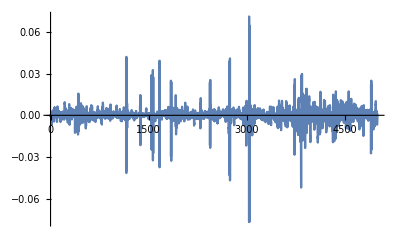

```mathematica
ListLinePlot[rsWethUsdc90dFilteredFirstMo, PlotRange->All]
```

```mathematica
edistWethUsdc90dFilteredLastMo
```

StableDistribution[1,1.58793,-0.0706768,-0.000101131,0.00135632]

```mathematica
edistWethUsdc90dFilteredFirstMo = EstimatedDistribution[rsWethUsdc90dFilteredFirstMo, StableDistribution[1, aWU90dFM, bWU90dFM, locWU90dFM, scaleWE90dFM]]
```

StableDistribution[1,1.42463,-0.0683195,0.0000414126,0.00174465]

```mathematica
(* Compare w last month *)
```

```mathematica
edistWethUsdc90dFilteredLastMo
```

StableDistribution[1,1.58793,-0.0706768,-0.000101131,0.00135632]

```mathematica
(* Similar but not completely exactly distributed. Ideally would have access to uncertainty in fit. scales are close tho which is good *)
```

```mathematica
(* TODO: Calc margin required given conditional prob breached level => want to min chance get to negative value position *)
```

```mathematica
(* Look at probabilities of different cap values being breached in t number of update periods into future. We use 10min here as our update period from the cron *)
```

```mathematica
(* C_p = e^{mu*t + sig*(t/a)^(1/a) * F^{-1}(1-alpha)} - 1 *)
```

```mathematica
Cp[t_,alpha_, a_, b_, mu_, sig_]:= Exp[mu*t +sig*(t/a)^(1/a)*InverseCDF[StableDistribution[1,a,b,0,1],1-alpha]]-1
```

```mathematica
sig[a_, scale_] :=scale/( 1/a)^(1/a)
```

```mathematica
mu[a_, loc_] := loc
```

```mathematica
alpha[t_, cp_, a_, b_, mu_, sig_]:= 1-CDF[StableDistribution[1,a,b,0,1],(Log[1+cp]-mu*t)/(sig*(t/a)^(1/a))]
```

```mathematica
(* Partial for wethusdc 90d params ... *)
```

```mathematica
edistWethUsdc90dFiltered
```

StableDistribution[1,1.46465,-0.0496207,-0.000010553,0.00154277]

```mathematica
mu[1.4646547203677354, -0.000010553047315527044]
```

-0.000010553

```mathematica
sig[1.4646547203677354, 0.0015427669619594313]
```

0.00200197

```mathematica
CpWethUsdc90dFiltered[t_, alpha_] := Cp[t, alpha,1.4646547203677354,  -0.04962071457296463, mu[1.4646547203677354, -0.000010553047315527044], sig[1.4646547203677354, 0.0015427669619594313]]
```

```mathematica
alphaWethUsdc90dFiltered[t_, cp_] := alpha[t,cp,1.4646547203677354,  -0.04962071457296463, mu[1.4646547203677354, -0.000010553047315527044], sig[1.4646547203677354, 0.0015427669619594313]]
```

```mathematica
(* for 10m update periods of cron, have 144 periods in 1d. *)
```

```mathematica
CpWethUsdc90dFiltered[144, 0.001]
```

4.55748

```mathematica
alphaWethUsdc90dFiltered[144, 4.55747500266425]
```

0.001

```mathematica
(* works :) *)
```

```mathematica
(* 99.9% of time on WETH/USDC, price won't increase 5.5x in a day *)
```

```mathematica
6*24
```

144

```mathematica
(* and for 7d ? *)
```

```mathematica
6*24*7
```

1008

```mathematica
CpWethUsdc90dFiltered[1008, 0.01]
```

3.03498

```mathematica
(* 99% of time on WETH/USDC, price won't increase 4x in a week *)
```

```mathematica
(* TODO: We have two time horizons to consider: 1. Cooldown on trading period (how often does this happen?); 2. Lookback rolling window to assess whether to cooldown ...  *)
```

```mathematica
(* ... 2. should be dictated by average time user is in a position so it's related to cap on payoff. 1. is related to inflation targets and OI definitive max to reach target *)
(* If we enforce Cp at certain level alpha over period t, then we should likely have t as the lookback window *)
```

```mathematica
CpWethUsdc90dFiltered[1008, 0.03]
```

1.03352

```mathematica
(* and for 14d ? *)
```

```mathematica
6*24*14
```

2016

```mathematica
CpWethUsdc90dFiltered[2016, 0.01]
```

8.34704

```mathematica
(* So: Assuming users immediately unwind once cap hits, a) only 1% of the time 9.34x cap will be breached over 2 week holding span; b) only 1% of the time 4.03x cap will be breached over 1 week holding span *)
```

```mathematica
(* But we want a relationship s.t. lower alpha stable a values produce lower cap in OI. If greater percent of time hit the Cp cap, counteract with lowering Coi accordingly. So e.g. if alpha jumps from 1% to 5% in frequency of breaching a 4x Cp cap, expected shortfall goes 5x assuming worst case OI amount and same OI cap for each case. We can therefore reduce the OI cap 1/5 to be inline. *)
```

```mathematica
(* This gives us the relationship we want: more intense tails, leads to more conservative markets => we take less risk by lowering OI cap *)
```

```mathematica
(* Then what's the function for determining alpha ? *)
```

```mathematica
alphaWethUsdc90dFiltered[144, 4.55747500266425]
```

0.001

```mathematica
alphaWethUsdc90dFiltered[1008,5]
```

0.00679635

```mathematica
alphaWethUsdc90dFiltered[2016,9]
```

0.009548

```mathematica
(* 5x within 1 week only happens 0.6% of time with WETH/USDC ... seems good *)
```

```mathematica
(* Check fit distribution over daily and weekly to see whether c is correct when extend: L_1 + L_2 = L_3 *)
```

```mathematica
tsWethUsdc90dFiltered = Table[tblWethUsdc90d[[i]][[2]], {i, 40, Length[tblWethUsdc90d]}]
```

{1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62245×10^9,1.62245×10^9,1.62245×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62468×10^9,1.62468×10^9,1.62468×10^9,1.62468×10^9,1.62468×10^9,1.62468×10^9,1.62468×10^9,1.62468×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62476×10^9,1.62476×10^9,1.62476×10^9,1.62476×10^9,1.62476×10^9,1.62476×10^9,1.62476×10^9,1.62476×10^9,1.62476×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62507×10^9,1.62507×10^9,1.62507×10^9,1.62507×10^9,1.62507×10^9,1.62507×10^9,1.62507×10^9}

```mathematica
tsWethUsdc90dFiltered
```

{1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61887×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61888×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.61889×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.6189×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61891×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61892×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61893×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61894×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61895×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61896×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61897×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61898×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.61899×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.619×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61901×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61902×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61903×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61904×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61905×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61906×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61907×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61908×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.61909×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.6191×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61911×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61912×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61913×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61914×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61915×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61916×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61917×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61918×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.61919×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.6192×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61921×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61922×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61923×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61924×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61925×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61926×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61927×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61928×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.61929×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.6193×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61931×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61932×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61933×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61934×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61935×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61936×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61937×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61938×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.61939×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.6194×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61941×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61942×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61943×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61944×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61945×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61946×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61947×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61948×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.61949×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.6195×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61951×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61952×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61953×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61954×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61955×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61956×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61957×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61958×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.61959×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.6196×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61961×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61962×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61963×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61964×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61965×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61966×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61967×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61968×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.61969×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.6197×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61971×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61972×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61973×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61974×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61975×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61976×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61977×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61978×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.61979×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.6198×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61981×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61982×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61983×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61984×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61985×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61986×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61987×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61988×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.61989×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.6199×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61991×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61992×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61993×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61994×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61995×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61996×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61997×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61998×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.61999×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62001×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62002×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62003×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62004×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62005×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62006×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62007×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62008×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.62009×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.6201×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62011×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62012×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62013×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62014×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62015×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62016×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62017×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62018×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.62019×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.6202×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62021×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62022×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62023×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62024×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62025×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62026×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62027×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62028×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.62029×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.6203×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62031×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62032×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62033×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62034×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62035×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62036×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62037×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62038×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.62039×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.6204×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62041×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62042×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62043×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62044×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62045×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62046×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62047×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62048×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.62049×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.6205×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62051×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62052×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62053×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62054×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62055×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62056×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62057×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62058×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.62059×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.6206×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62061×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62062×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62063×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62064×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62065×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62066×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62067×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62068×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.62069×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.6207×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62071×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62072×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62073×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62074×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62075×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62076×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62077×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62078×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.62079×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.6208×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62081×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62082×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62083×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62084×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62085×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62086×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62087×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62088×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.62089×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.6209×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62091×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62092×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62093×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62094×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62095×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62096×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62097×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62098×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.62099×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.621×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62101×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62102×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62103×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62104×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62105×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62106×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62107×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62108×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.62109×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.6211×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62111×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62112×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62113×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62114×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62115×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62116×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62117×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62118×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.62119×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.6212×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62121×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62122×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62123×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62124×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62125×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62126×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62127×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62128×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.62129×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.6213×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62131×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62132×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62133×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62134×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62135×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62136×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62137×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62138×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.62139×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.6214×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62141×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62142×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62143×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62144×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62145×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62146×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62147×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62148×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.62149×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.6215×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62151×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62152×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62153×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62154×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62155×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62156×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62157×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62158×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.62159×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.6216×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62161×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62162×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62163×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62164×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62165×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62166×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62167×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62168×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.62169×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.6217×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62171×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62172×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62173×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62174×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62175×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62176×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62177×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62178×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.62179×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.6218×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62181×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62182×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62183×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62184×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62185×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62186×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62187×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62188×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.62189×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.6219×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62191×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62192×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62193×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62194×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62195×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62196×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62197×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62198×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.62199×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.622×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62201×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62202×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62203×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62204×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62205×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62206×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62207×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62208×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.62209×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.6221×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62211×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62212×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62213×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62214×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62215×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62216×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62217×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62218×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.62219×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.6222×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62221×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62222×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62223×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62224×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62225×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62226×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62227×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62228×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.62229×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.6223×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62231×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62232×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62233×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62234×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62235×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62236×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62237×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62238×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.62239×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.6224×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62241×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62242×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62243×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62244×10^9,1.62245×10^9,1.62245×10^9,1.62245×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62251×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62252×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62253×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62254×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62255×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62256×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62257×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62258×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.62259×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.6226×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62261×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62262×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62263×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62264×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62265×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62266×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62267×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62268×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.62269×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.6227×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62271×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62272×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62273×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62274×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62275×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62276×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62277×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62278×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.62279×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.6228×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62281×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62282×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62283×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62284×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62285×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62286×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62287×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62288×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.62289×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.6229×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62291×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62292×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62293×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62294×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62295×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62296×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62297×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62298×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.62299×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.623×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62301×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62302×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62303×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62304×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62305×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62306×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62307×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62308×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.62309×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.6231×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62311×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62312×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62313×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62314×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62315×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62316×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62317×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62318×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.62319×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.6232×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62321×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62322×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62323×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62324×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62325×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62326×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62327×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62328×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.62329×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.6233×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62331×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62332×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62333×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62334×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62335×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62336×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62337×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62338×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.62339×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.6234×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62341×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62342×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62343×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62344×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62345×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62346×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62347×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62348×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.62349×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.6235×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62351×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62352×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62353×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62354×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62355×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62356×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62357×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62358×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.62359×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.6236×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62361×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62362×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62363×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62364×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62365×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62366×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62367×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62368×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.62369×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.6237×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62371×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62372×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62373×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62374×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62375×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62376×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62377×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62378×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.62379×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.6238×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62381×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62382×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62383×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62384×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62385×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62386×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62387×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62388×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.62389×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.6239×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62391×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62392×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62393×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62394×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62395×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62396×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62397×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62398×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.62399×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.624×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62401×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62402×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62403×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62404×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62405×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62406×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62407×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62408×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.62409×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.6241×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62411×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62412×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62413×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62414×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62415×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62416×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62417×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62418×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.62419×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.6242×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62421×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62422×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62423×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62424×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62425×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62426×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62427×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62428×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.62429×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.6243×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62431×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62432×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62433×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62434×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62435×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62436×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62437×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62438×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.62439×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.6244×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62441×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62442×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62443×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62444×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62445×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62446×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62447×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62448×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.62449×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.6245×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62451×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62452×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62453×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62454×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62455×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62456×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62457×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62458×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.62459×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.6246×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62461×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62462×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62463×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62464×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62465×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62466×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62467×10^9,1.62468×10^9,1.62468×10^9,1.62468×10^9,1.62468×10^9,1.62468×10^9,1.62468×10^9,1.62468×10^9,1.62468×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.62469×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.6247×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62471×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62472×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62473×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62474×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62475×10^9,1.62476×10^9,1.62476×10^9,1.62476×10^9,1.62476×10^9,1.62476×10^9,1.62476×10^9,1.62476×10^9,1.62476×10^9,1.62476×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62477×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62478×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.62479×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.6248×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62481×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62482×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62483×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62484×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62485×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62486×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62487×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62488×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.62489×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.6249×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62491×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62492×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62493×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62494×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62495×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62496×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62497×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62498×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.62499×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.625×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62501×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62502×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62503×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62504×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62505×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62506×10^9,1.62507×10^9,1.62507×10^9,1.62507×10^9,1.62507×10^9,1.62507×10^9,1.62507×10^9,1.62507×10^9}

```mathematica
dtsWethUsdc90dFiltered = Differences[tsWethUsdc90dFiltered]
```

{876.,703.,681.,609.,594.,755.,642.,635.,620.,694.,599.,681.,734.,661.,607.,737.,685.,667.,554.,740.,563.,570.,847.,461.,902.,583.,699.,667.,657.,621.,656.,540.,746.,527.,678.,730.,541.,707.,694.,605.,644.,549.,578.,651.,836.,598.,707.,654.,465.,653.,600.,890.,509.,698.,540.,904.,644.,646.,535.,674.,678.,428.,921.,389.,868.,679.,696.,561.,734.,647.,625.,498.,796.,711.,533.,526.,745.,702.,419.,870.,718.,464.,416.,803.,721.,742.,736.,673.,622.,559.,801.,649.,628.,587.,610.,697.,571.,641.,974.,581.,658.,759.,609.,827.,854.,579.,776.,586.,660.,724.,279.,1001.,698.,581.,734.,392.,901.,622.,675.,596.,710.,556.,781.,632.,712.,600.,662.,754.,392.,850.,620.,565.,603.,840.,642.,593.,626.,682.,476.,797.,630.,730.,544.,763.,208.,620.,886.,821.,606.,657.,656.,503.,786.,635.,440.,835.,369.,544.,1043.,358.,874.,696.,110.,1133.,627.,720.,189.,1029.,578.,769.,652.,569.,777.,613.,572.,659.,683.,651.,588.,760.,631.,653.,637.,481.,721.,690.,657.,485.,756.,710.,639.,552.,653.,654.,637.,500.,791.,654.,507.,867.,652.,583.,574.,742.,617.,717.,573.,692.,528.,762.,645.,580.,734.,610.,651.,660.,554.,595.,506.,913.,630.,461.,663.,820.,640.,659.,493.,801.,612.,684.,656.,432.,853.,689.,622.,470.,830.,638.,530.,760.,865.,662.,419.,942.,765.,637.,773.,724.,462.,821.,775.,538.,646.,792.,690.,624.,710.,512.,714.,571.,597.,537.,954.,544.,785.,419.,638.,589.,938.,693.,623.,661.,418.,870.,672.,654.,629.,620.,707.,406.,923.,483.,755.,677.,669.,542.,713.,730.,647.,549.,724.,666.,679.,611.,611.,1185.,730.,638.,697.,697.,699.,628.,547.,732.,675.,623.,641.,251.,972.,709.,495.,810.,563.,727.,696.,483.,728.,621.,561.,806.,565.,594.,802.,658.,654.,616.,595.,700.,643.,632.,569.,718.,582.,716.,584.,720.,620.,559.,688.,691.,549.,630.,669.,755.,724.,607.,660.,636.,713.,517.,758.,656.,681.,664.,642.,696.,578.,724.,662.,729.,331.,1008.,635.,689.,710.,688.,710.,657.,589.,1989.,860.,616.,701.,595.,777.,684.,601.,612.,658.,678.,652.,591.,585.,788.,627.,509.,665.,777.,605.,628.,678.,652.,645.,643.,642.,666.,612.,688.,619.,667.,583.,633.,718.,532.,773.,625.,669.,727.,537.,495.,919.,656.,638.,644.,681.,692.,704.,676.,656.,652.,647.,572.,701.,622.,697.,655.,640.,600.,517.,810.,656.,663.,632.,656.,702.,702.,678.,635.,712.,663.,660.,640.,665.,704.,531.,699.,722.,672.,647.,608.,640.,683.,642.,676.,642.,682.,737.,687.,678.,801.,690.,666.,670.,682.,599.,758.,513.,821.,612.,569.,866.,617.,649.,423.,890.,791.,709.,710.,623.,703.,573.,741.,678.,467.,973.,713.,690.,581.,713.,582.,858.,577.,761.,674.,681.,749.,675.,666.,696.,518.,894.,608.,1330.,418.,913.,616.,663.,665.,633.,516.,444.,699.,918.,669.,679.,638.,640.,540.,755.,492.,811.,637.,610.,750.,604.,625.,472.,738.,575.,370.,1068.,737.,620.,646.,591.,676.,751.,658.,636.,631.,671.,562.,641.,775.,670.,249.,1112.,653.,666.,556.,716.,680.,619.,647.,463.,839.,453.,948.,654.,463.,771.,706.,704.,554.,759.,698.,526.,740.,702.,301.,954.,777.,663.,590.,641.,568.,776.,741.,680.,623.,716.,538.,682.,446.,875.,619.,413.,691.,905.,661.,715.,676.,507.,774.,653.,720.,623.,743.,470.,800.,651.,701.,552.,759.,646.,670.,621.,209.,1065.,159.,1267.,551.,659.,742.,668.,675.,702.,562.,808.,680.,653.,672.,504.,818.,659.,691.,691.,706.,716.,457.,804.,779.,587.,682.,749.,1015.,679.,723.,635.,682.,719.,718.,573.,784.,626.,672.,815.,644.,603.,548.,580.,965.,696.,657.,709.,700.,685.,440.,595.,892.,607.,555.,488.,775.,738.,731.,501.,758.,281.,999.,653.,643.,639.,659.,567.,515.,752.,608.,510.,776.,722.,613.,735.,638.,660.,548.,671.,553.,797.,520.,563.,789.,722.,645.,640.,635.,665.,552.,721.,421.,836.,722.,468.,808.,490.,797.,623.,640.,489.,810.,630.,650.,610.,711.,517.,755.,601.,598.,735.,671.,625.,682.,581.,615.,587.,749.,519.,704.,429.,981.,625.,619.,660.,558.,574.,790.,705.,599.,543.,761.,538.,714.,639.,630.,721.,602.,691.,294.,788.,892.,645.,672.,558.,663.,633.,645.,579.,721.,690.,520.,733.,691.,635.,643.,673.,525.,758.,561.,764.,522.,741.,571.,812.,637.,703.,482.,793.,692.,608.,665.,633.,690.,651.,609.,715.,656.,622.,647.,527.,705.,707.,672.,682.,558.,601.,799.,671.,570.,611.,736.,635.,676.,578.,660.,692.,660.,590.,674.,626.,603.,679.,721.,651.,623.,654.,623.,707.,680.,576.,690.,479.,793.,682.,446.,783.,415.,919.,573.,695.,691.,635.,658.,678.,420.,589.,892.,605.,651.,606.,797.,576.,815.,708.,591.,665.,585.,737.,727.,728.,371.,903.,718.,548.,681.,623.,681.,726.,617.,773.,646.,693.,474.,673.,758.,712.,561.,628.,830.,711.,651.,528.,765.,840.,632.,690.,632.,636.,353.,1042.,771.,667.,478.,870.,719.,694.,689.,536.,515.,957.,457.,856.,656.,679.,714.,600.,758.,658.,533.,735.,795.,661.,1194.,655.,630.,515.,619.,958.,561.,709.,773.,621.,682.,564.,720.,658.,630.,552.,765.,651.,677.,639.,587.,786.,497.,798.,537.,733.,554.,744.,639.,403.,815.,638.,716.,433.,803.,666.,639.,612.,733.,491.,540.,866.,521.,599.,723.,722.,444.,811.,702.,375.,945.,581.,729.,688.,574.,480.,862.,550.,706.,488.,728.,755.,499.,668.,545.,843.,583.,746.,625.,661.,612.,627.,671.,428.,837.,443.,581.,864.,661.,712.,647.,162.,925.,744.,664.,567.,594.,676.,750.,572.,786.,638.,624.,554.,700.,730.,663.,369.,932.,664.,674.,654.,775.,380.,887.,573.,750.,641.,536.,652.,870.,506.,746.,710.,603.,612.,709.,622.,673.,662.,534.,717.,594.,724.,652.,628.,693.,562.,822.,668.,636.,635.,701.,685.,620.,675.,891.,691.,710.,789.,605.,823.,625.,728.,672.,626.,770.,773.,590.,802.,653.,594.,749.,544.,862.,669.,605.,671.,735.,763.,688.,527.,569.,831.,827.,615.,781.,721.,677.,692.,732.,658.,712.,711.,689.,641.,578.,763.,526.,776.,593.,523.,920.,705.,702.,592.,608.,809.,207.,987.,767.,519.,717.,472.,793.,718.,652.,642.,529.,757.,645.,551.,761.,721.,596.,503.,801.,826.,606.,692.,789.,692.,676.,672.,533.,667.,779.,659.,544.,685.,714.,253.,1169.,548.,546.,841.,637.,656.,684.,621.,559.,790.,449.,917.,502.,867.,635.,660.,702.,487.,875.,610.,699.,666.,587.,697.,660.,666.,535.,493.,963.,541.,810.,534.,718.,651.,677.,687.,713.,649.,618.,773.,592.,814.,667.,1021.,614.,629.,609.,717.,708.,695.,646.,607.,690.,665.,612.,669.,724.,609.,659.,595.,672.,657.,525.,692.,803.,679.,648.,494.,629.,694.,706.,677.,650.,566.,737.,589.,659.,576.,791.,667.,605.,630.,764.,636.,517.,715.,741.,567.,665.,684.,570.,769.,623.,605.,373.,909.,672.,786.,670.,579.,770.,638.,680.,494.,667.,774.,534.,751.,664.,660.,668.,562.,702.,706.,724.,550.,630.,705.,604.,720.,622.,665.,702.,705.,504.,864.,584.,743.,540.,783.,682.,688.,690.,636.,481.,954.,723.,673.,645.,646.,595.,652.,633.,908.,686.,560.,717.,558.,784.,613.,706.,473.,756.,747.,644.,665.,561.,692.,658.,707.,547.,763.,634.,754.,556.,763.,508.,697.,681.,636.,465.,889.,611.,599.,649.,641.,698.,970.,892.,688.,663.,634.,685.,652.,685.,712.,625.,737.,463.,864.,644.,618.,706.,650.,555.,393.,798.,743.,731.,430.,849.,527.,770.,599.,585.,831.,594.,523.,915.,630.,666.,500.,769.,613.,665.,735.,668.,489.,741.,679.,559.,796.,681.,678.,610.,645.,632.,618.,795.,476.,686.,777.,649.,517.,595.,845.,579.,725.,596.,670.,560.,711.,541.,701.,594.,704.,723.,596.,654.,559.,739.,563.,579.,789.,618.,690.,613.,633.,656.,609.,608.,747.,642.,611.,560.,596.,835.,684.,582.,703.,656.,673.,546.,756.,677.,650.,528.,853.,619.,622.,725.,648.,607.,570.,754.,584.,752.,536.,709.,498.,754.,706.,53.,1228.,683.,661.,633.,549.,523.,548.,862.,767.,663.,512.,580.,850.,699.,625.,730.,640.,860.,626.,669.,621.,592.,734.,219.,870.,555.,774.,809.,513.,612.,758.,644.,508.,647.,844.,224.,1140.,565.,664.,705.,631.,648.,560.,779.,641.,658.,602.,520.,774.,687.,648.,587.,696.,478.,496.,942.,578.,582.,772.,614.,514.,882.,686.,619.,676.,620.,544.,862.,315.,975.,576.,669.,743.,235.,1062.,662.,653.,699.,652.,591.,724.,738.,647.,626.,559.,599.,786.,612.,719.,674.,626.,682.,643.,647.,573.,752.,642.,676.,642.,540.,774.,711.,560.,713.,632.,692.,610.,701.,619.,663.,700.,597.,643.,726.,659.,586.,742.,566.,808.,660.,612.,670.,639.,632.,690.,757.,611.,606.,787.,645.,665.,636.,587.,711.,542.,827.,596.,739.,343.,951.,613.,622.,681.,752.,659.,627.,742.,677.,681.,557.,792.,1297.,565.,755.,570.,301.,1061.,510.,744.,608.,686.,711.,690.,484.,823.,666.,659.,526.,569.,690.,808.,642.,607.,619.,690.,585.,720.,582.,590.,664.,722.,650.,479.,822.,643.,566.,946.,1590.,1595.,617.,695.,668.,547.,746.,460.,498.,998.,561.,646.,716.,531.,687.,714.,541.,733.,562.,635.,536.,774.,645.,649.,671.,538.,579.,784.,652.,625.,586.,634.,653.,616.,619.,724.,622.,689.,638.,535.,631.,678.,710.,655.,514.,794.,161.,1116.,637.,502.,653.,628.,715.,687.,575.,661.,684.,658.,607.,726.,492.,551.,766.,594.,635.,748.,609.,580.,777.,632.,747.,587.,680.,836.,629.,816.,660.,674.,737.,613.,707.,680.,678.,780.,662.,684.,732.,750.,657.,632.,657.,726.,665.,656.,956.,685.,644.,479.,781.,682.,628.,423.,877.,497.,819.,608.,660.,682.,687.,541.,718.,477.,842.,593.,691.,561.,647.,737.,554.,388.,925.,496.,770.,741.,583.,275.,1069.,651.,631.,642.,220.,1085.,678.,611.,502.,824.,559.,709.,639.,703.,498.,811.,550.,546.,757.,657.,639.,695.,618.,544.,772.,582.,577.,722.,639.,560.,705.,661.,619.,471.,701.,801.,615.,666.,655.,550.,683.,529.,760.,593.,642.,736.,376.,812.,604.,750.,595.,726.,632.,634.,440.,827.,713.,658.,523.,712.,592.,720.,650.,587.,641.,604.,758.,631.,724.,671.,517.,740.,680.,584.,691.,689.,669.,654.,594.,692.,604.,637.,670.,609.,602.,747.,646.,664.,491.,701.,755.,657.,596.,698.,666.,634.,559.,769.,664.,458.,819.,645.,680.,616.,940.,632.,683.,629.,642.,684.,622.,679.,573.,622.,741.,643.,637.,606.,641.,682.,642.,662.,648.,630.,698.,690.,616.,668.,634.,665.,517.,753.,655.,643.,590.,732.,557.,727.,509.,794.,661.,654.,652.,585.,685.,620.,720.,666.,611.,654.,648.,594.,698.,596.,603.,524.,801.,703.,566.,721.,663.,645.,634.,478.,803.,640.,656.,688.,541.,718.,576.,701.,585.,672.,713.,611.,615.,671.,695.,529.,757.,605.,618.,407.,976.,681.,621.,715.,652.,677.,618.,745.,1489.,694.,677.,699.,683.,685.,641.,756.,722.,683.,673.,717.,665.,592.,657.,746.,820.,672.,669.,569.,770.,695.,672.,1133.,733.,634.,527.,786.,634.,478.,748.,731.,595.,702.,601.,663.,534.,835.,562.,510.,911.,309.,889.,663.,746.,617.,848.,690.,620.,730.,447.,946.,609.,581.,719.,722.,660.,672.,508.,578.,918.,664.,636.,702.,336.,936.,1322.,705.,644.,707.,630.,636.,665.,677.,600.,696.,628.,662.,577.,599.,737.,638.,711.,666.,658.,699.,581.,581.,744.,674.,622.,1394.,696.,408.,741.,809.,647.,582.,596.,716.,693.,594.,680.,685.,521.,722.,672.,644.,595.,721.,557.,428.,796.,735.,652.,710.,612.,754.,506.,600.,848.,692.,558.,737.,721.,648.,625.,737.,574.,508.,816.,685.,749.,279.,1090.,691.,594.,657.,787.,559.,775.,657.,679.,607.,745.,502.,772.,504.,875.,472.,921.,658.,629.,805.,535.,619.,798.,539.,684.,449.,921.,630.,691.,566.,1400.,272.,1008.,646.,596.,739.,594.,555.,553.,730.,797.,593.,606.,750.,634.,636.,676.,637.,707.,561.,710.,630.,617.,645.,703.,450.,803.,655.,665.,740.,667.,608.,619.,741.,649.,673.,651.,692.,562.,707.,573.,757.,820.,633.,675.,757.,207.,1141.,740.,638.,762.,690.,294.,1088.,580.,771.,761.,575.,788.,428.,979.,676.,698.,733.,599.,768.,633.,782.,640.,558.,801.,603.,798.,784.,690.,565.,788.,692.,710.,672.,514.,906.,692.,687.,660.,488.,926.,745.,563.,827.,598.,743.,718.,706.,636.,649.,728.,309.,1028.,781.,739.,710.,609.,703.,722.,712.,548.,836.,746.,642.,679.,783.,615.,661.,654.,843.,1136.,703.,655.,580.,675.,627.,1326.,623.,641.,519.,729.,677.,665.,617.,370.,898.,468.,789.,648.,544.,698.,708.,673.,636.,427.,767.,721.,561.,656.,680.,661.,608.,693.,296.,531.,1084.,672.,569.,610.,565.,725.,638.,712.,653.,657.,500.,781.,590.,541.,719.,673.,702.,645.,530.,727.,634.,645.,594.,674.,555.,700.,688.,599.,659.,682.,578.,634.,667.,634.,693.,520.,714.,676.,647.,539.,628.,751.,514.,578.,811.,651.,583.,681.,618.,660.,595.,685.,683.,607.,637.,659.,674.,588.,665.,652.,550.,518.,777.,703.,598.,673.,632.,475.,566.,442.,992.,682.,654.,683.,635.,625.,499.,714.,653.,585.,761.,670.,662.,639.,479.,773.,397.,847.,706.,444.,776.,673.,596.,677.,608.,650.,687.,613.,686.,1157.,629.,727.,650.,651.,717.,542.,711.,668.,634.,576.,640.,655.,744.,559.,656.,598.,765.,504.,759.,655.,642.,662.,709.,591.,681.,550.,735.,677.,653.,642.,676.,565.,712.,650.,496.,1489.,734.,414.,885.,624.,483.,850.,619.,610.,721.,575.,698.,621.,709.,522.,491.,714.,789.,663.,659.,606.,723.,454.,639.,865.,662.,691.,518.,699.,600.,742.,673.,663.,617.,537.,791.,702.,526.,732.,279.,1106.,588.,758.,527.,487.,946.,713.,283.,1070.,643.,476.,520.,902.,589.,630.,880.,560.,813.,663.,741.,687.,674.,593.,677.,732.,677.,667.,711.,722.,683.,584.,748.,664.,740.,730.,668.,625.,742.,599.,729.,604.,822.,784.,675.,525.,821.,617.,737.,607.,612.,698.,721.,538.,882.,656.,386.,947.,505.,840.,519.,829.,616.,604.,607.,711.,685.,660.,1255.,657.,643.,1296.,565.,697.,611.,592.,675.,642.,657.,566.,769.,560.,641.,661.,290.,938.,380.,1020.,359.,902.,617.,597.,736.,435.,807.,563.,711.,593.,712.,607.,704.,649.,620.,727.,524.,648.,764.,597.,593.,698.,649.,35.,1176.,749.,571.,521.,683.,761.,585.,530.,733.,553.,377.,1026.,629.,501.,804.,483.,463.,885.,699.,608.,817.,662.,601.,302.,903.,700.,517.,565.,890.,654.,574.,722.,562.,710.,613.,752.,326.,953.,659.,513.,743.,620.,701.,528.,758.,487.,814.,655.,600.,301.,1054.,683.,612.,695.,568.,675.,564.,752.,647.,677.,630.,597.,662.,519.,728.,583.,522.,862.,618.,622.,722.,1309.,651.,155.,916.,838.,715.,874.,665.,637.,638.,628.,666.,652.,661.,534.,732.,427.,822.,641.,550.,389.,954.,557.,593.,725.,746.,587.,621.,643.,688.,635.,553.,670.,550.,663.,676.,670.,586.,588.,733.,664.,651.,660.,603.,407.,896.,326.,744.,775.,691.,700.,617.,606.,690.,493.,708.,473.,824.,696.,702.,655.,573.,715.,656.,696.,380.,904.,368.,922.,701.,497.,787.,674.,632.,528.,725.,756.,544.,597.,770.,145.,1236.,704.,610.,455.,909.,610.,679.,450.,877.,455.,860.,525.,1456.,583.,622.,719.,399.,494.,1080.,695.,658.,695.,537.,673.,709.,590.,718.,717.,443.,360.,1149.,698.,518.,709.,780.,571.,760.,588.,720.,511.,792.,710.,690.,592.,628.,787.,521.,775.,658.,683.,659.,624.,677.,694.,655.,659.,655.,692.,1317.,781.,757.,727.,577.,820.,611.,863.,673.,654.,668.,573.,781.,720.,827.,629.,775.,632.,701.,546.,837.,518.,722.,763.,694.,732.,716.,596.,807.,533.,825.,612.,683.,766.,646.,652.,848.,638.,713.,573.,815.,695.,720.,436.,747.,641.,857.,673.,804.,1241.,579.,515.,814.,567.,321.,1004.,551.,773.,681.,545.,247.,1164.,500.,799.,681.,667.,550.,897.,433.,892.,749.,685.,534.,625.,859.,553.,749.,766.,677.,611.,736.,678.,721.,724.,388.,858.,866.,653.,854.,240.,1014.,878.,768.,618.,640.,839.,656.,773.,520.,878.,637.,674.,638.,662.,1409.,613.,610.,600.,688.,720.,402.,717.,851.,609.,490.,836.,565.,660.,722.,525.,779.,521.,790.,566.,318.,1062.,678.,418.,1052.,650.,696.,669.,603.,943.,436.,903.,595.,518.,865.,626.,938.,622.,720.,700.,664.,1359.,529.,887.,664.,630.,766.,692.,699.,584.,707.,762.,653.,653.,707.,720.,594.,684.,593.,814.,591.,786.,372.,956.,712.,708.,625.,747.,429.,890.,733.,596.,725.,443.,871.,1313.,622.,324.,1028.,586.,698.,670.,670.,690.,619.,678.,526.,820.,630.,655.,709.,658.,683.,543.,648.,679.,714.,734.,744.,468.,421.,1085.,741.,627.,685.,687.,680.,582.,818.,530.,632.,868.,1406.,652.,638.,752.,669.,643.,694.,630.,654.,750.,613.,674.,562.,594.,825.,647.,678.,665.,668.,507.,788.,354.,840.,715.,622.,493.,835.,462.,797.,737.,558.,753.,676.,560.,732.,654.,738.,659.,1468.,632.,692.,649.,641.,751.,639.,662.,646.,665.,618.,676.,666.,643.,627.,704.,608.,650.,694.,493.,708.,721.,515.,739.,697.,609.,599.,677.,643.,659.,601.,599.,706.,868.,673.,611.,743.,578.,716.,731.,474.,829.,643.,696.,627.,680.,735.,655.,653.,583.,839.,580.,571.,787.,709.,763.,700.,754.,701.,639.,733.,727.,703.,726.,705.,722.,718.,567.,861.,670.,522.,899.,724.,591.,804.,672.,607.,740.,640.,717.,813.,695.,685.,661.,810.,654.,720.,701.,611.,806.,726.,688.,690.,641.,736.,689.,782.,544.,841.,705.,617.,694.,735.,657.,685.,588.,724.,646.,660.,562.,759.,662.,740.,659.,683.,567.,736.,411.,889.,580.,591.,699.,756.,613.,661.,587.,726.,621.,627.,684.,613.,513.,784.,678.,549.,809.,648.,618.,410.,896.,659.,689.,612.,737.,457.,713.,678.,728.,610.,503.,806.,633.,659.,612.,704.,642.,577.,612.,819.,649.,655.,571.,664.,584.,633.,931.,589.,671.,604.,693.,250.,999.,703.,631.,550.,760.,563.,631.,601.,592.,836.,1306.,682.,595.,582.,755.,407.,893.,585.,410.,836.,477.,824.,702.,424.,904.,268.,1012.,564.,697.,606.,784.,690.,622.,787.,452.,806.,718.,635.,798.,761.,572.,678.,796.,633.,699.,671.,742.,696.,723.,783.,699.,801.,627.,739.,789.,674.,668.,763.,790.,702.,650.,427.,913.,786.,449.,891.,689.,527.,925.,669.,739.,720.,677.,706.,692.,705.,716.,495.,886.,616.,857.,634.,709.,560.,813.,692.,614.,475.,817.,691.,654.,667.,559.,751.,617.,611.,728.,520.,772.,292.,887.,681.,536.,737.,372.,819.,848.,563.,736.,523.,764.,652.,647.,651.,612.,879.,860.,630.,672.,675.,648.,530.,714.,417.,826.,723.,618.,1203.,736.,478.,907.,633.,716.,690.,180.,1087.,763.,640.,705.,610.,756.,530.,636.,923.,547.,760.,712.,592.,771.,691.,440.,696.,781.,698.,459.,659.,873.,813.,633.,709.,443.,919.,770.,547.,801.,733.,684.,716.,680.,641.,751.,644.,746.,624.,599.,865.,583.,768.,711.,739.,625.,742.,743.,623.,739.,666.,723.,696.,697.,694.,654.,629.,618.,824.,714.,623.,779.,612.,722.,706.,724.,605.,675.,763.,549.,837.,686.,432.,923.,719.,577.,678.,777.,717.,668.,732.,717.,732.,655.,713.,695.,695.,716.,653.,728.,545.,867.,749.,420.,587.,876.,862.,577.,780.,672.,632.,602.,761.,747.,577.,883.,620.,515.,676.,760.,682.,646.,597.,702.,599.,572.,793.,1338.,588.,629.,835.,287.,696.,1007.,484.,858.,630.,624.,712.,603.,693.,659.,582.,739.,349.,781.,706.,584.,735.,481.,844.,521.,785.,493.,647.,823.,627.,612.,495.,848.,566.,631.,693.,624.,626.,698.,503.,795.,688.,678.,490.,774.,675.,660.,554.,673.,672.,656.,648.,555.,706.,610.,697.,574.,706.,649.,614.,664.,565.,726.,675.,609.,635.,712.,585.,677.,698.,626.,609.,587.,671.,596.,753.,567.,719.,645.,616.,678.,678.,654.,627.,633.,645.,657.,576.,665.,621.,542.,850.,537.,697.,598.,722.,561.,759.,551.,734.,655.,506.,833.,564.,751.,560.,671.,695.,610.,633.,650.,560.,717.,785.,673.,675.,662.,681.,651.,697.,630.,676.,682.,680.,625.,715.,636.,645.,669.,663.,381.,828.,823.,710.,666.,1145.,759.,738.,557.,639.,766.,648.,271.,901.,755.,582.,495.,768.,707.,682.,713.,654.,662.,660.,649.,643.,675.,727.,671.,593.,736.,710.,657.,737.,711.,712.,681.,688.,646.,688.,716.,758.,691.,581.,746.,664.,702.,669.,695.,740.,622.,745.,631.,766.,655.,700.,648.,788.,683.,742.,769.,725.,694.,679.,706.,615.,249.,990.,678.,699.,674.,701.,655.,664.,659.,667.,616.,582.,731.,241.,1066.,640.,656.,673.,627.,644.,625.,724.,623.,655.,634.,670.,679.,635.,753.,716.,582.,766.,547.,797.,685.,635.,696.,654.,557.,796.,585.,732.,496.,796.,714.,643.,645.,655.,696.,614.,689.,662.,697.,632.,658.,652.,671.,649.,677.,650.,716.,707.,672.,653.,612.,709.,667.,526.,1368.,662.,796.,668.,624.,579.,783.,694.,591.,714.,694.,674.,680.,670.,666.,642.,711.,669.,617.,666.,581.,744.,661.,688.,660.,771.,638.,690.,661.,694.,674.,635.,678.,723.,644.,709.,644.,713.,645.,704.,709.,615.,718.,617.,771.,595.,821.,862.,733.,652.,706.,779.,723.,654.,474.,898.,620.,640.,729.,491.,806.,679.,574.,504.,804.,716.,626.,634.,626.,748.,693.,387.,846.,756.,638.,592.,748.,681.,656.,984.,685.,643.,553.,707.,619.,671.,683.,550.,623.,526.,867.,656.,626.,670.,647.,657.,653.,566.,714.,593.,694.,652.,601.,664.,669.,429.,679.,716.,708.,633.,653.,656.,653.,641.,608.,643.,686.,648.,626.,670.,683.,639.,598.,718.,592.,703.,647.,687.,623.,674.,657.,640.,671.,652.,645.,546.,734.,673.,616.,581.,746.,535.,788.,667.,632.,631.,668.,586.,701.,638.,678.,598.,684.,632.,646.,689.,658.,611.,677.,646.,609.,704.,666.,661.,669.,612.,685.,757.,685.,677.,657.,675.,689.,1428.,1038.,684.,682.,608.,638.,650.,717.,621.,687.,669.,618.,650.,623.,654.,621.,703.,617.,712.,1459.,1028.,583.,731.,652.,262.,362.,777.,713.,615.,690.,688.,620.,714.,681.,635.,583.,722.,641.,654.,739.,632.,670.,650.,632.,635.,703.,645.,667.,637.,675.,671.,653.,667.,709.,643.,710.,615.,626.,741.,708.,628.,658.,669.,1538.,719.,640.,677.,690.,663.,758.,702.,661.,686.,634.,680.,759.,755.,667.,675.,706.,724.,699.,716.,693.,759.,666.,602.,655.,806.,677.,701.,649.,724.,662.,691.,725.,700.,655.,777.,687.,741.,754.,544.,859.,651.,741.,565.,785.,719.,662.,685.,785.,700.,710.,715.,596.,809.,727.,733.,704.,701.,634.,783.,641.,767.,732.,634.,699.,746.,613.,702.,746.,673.,592.,776.,695.,690.,701.,746.,686.,710.,672.,713.,697.,686.,718.,600.,812.,632.,737.,712.,686.,724.,791.,701.,699.,755.,677.,765.,693.,672.,753.,634.,731.,698.,875.,713.,767.,712.,686.,740.,668.,818.,635.,647.,733.,757.,751.,627.,609.,778.,721.,637.,760.,649.,782.,770.,726.,751.,582.,709.,729.,629.,708.,586.,732.,625.,607.,753.,608.,616.,714.,608.,651.,710.,631.,682.,655.,635.,623.,659.,692.,627.,564.,733.,580.,727.,455.,790.,718.,628.,688.,844.,602.,840.,771.,684.,740.,588.,839.,672.,698.,806.,585.,783.,619.,630.,720.,593.,705.,707.,631.,681.,713.,687.,708.,675.,788.,647.,663.,666.,653.,711.,628.,717.,663.,619.,701.,709.,587.,720.,717.,665.,658.,692.,381.,966.,689.,630.,643.,670.,703.,694.,631.,685.,645.,641.,698.,665.,612.,738.,657.,570.,786.,620.,659.,692.,650.,651.,701.,645.,645.,608.,744.,718.,675.,655.,590.,641.,701.,719.,603.,739.,637.,610.,700.,631.,618.,726.,704.,655.,675.,589.,730.,676.,743.,698.,689.,653.,710.,685.,699.,665.,691.,603.,777.,685.,702.,668.,638.,724.,655.,589.,737.,703.,667.,537.,803.,670.,721.,642.,674.,703.,578.,718.,745.,730.,638.,653.,688.,726.,673.,704.,583.,619.,739.,584.,663.,665.,581.,616.,672.,713.,752.,624.,615.,649.,707.,663.,652.,655.,703.,552.,732.,689.,653.,682.,716.,661.,659.,559.,679.,747.,548.,799.,606.,677.,667.,652.,684.,659.,668.,608.,709.,544.,750.,650.,599.,717.,625.,665.,595.,711.,616.,674.,630.,705.,632.,662.,574.,748.,579.,697.,622.,649.,699.,632.,640.,528.,806.,583.,541.,803.,647.,620.,666.,651.,681.,543.,692.,714.,633.,638.,644.,664.,614.,632.,644.,586.,744.,539.,734.,591.,737.,624.,601.,752.,646.,578.,654.,730.,623.,658.,432.,879.,604.,614.,739.,593.,704.,652.,670.,660.,630.,648.,643.,680.,596.,661.,662.,626.,661.,634.,630.,658.,630.,675.,610.,672.,584.,657.,686.,680.,626.,892.,624.,644.,638.,725.,622.,691.,648.,627.,679.,658.,665.,619.,698.,663.,647.,615.,706.,755.,674.,616.,682.,627.,648.,645.,626.,671.,665.,627.,660.,657.,656.,616.,675.,635.,644.,665.,651.,638.,637.,632.,649.,635.,639.,684.,608.,662.,625.,629.,577.,730.,654.,662.,632.,602.,715.,641.,666.,615.,664.,553.,693.,534.,795.,631.,686.,600.,649.,613.,683.,640.,666.,641.,624.,676.,645.,648.,659.,700.,631.,648.,702.,633.,689.,700.,680.,570.,806.,711.,626.,691.,704.,660.,642.,726.,669.,662.,676.,676.,671.,627.,729.,720.,723.,545.,722.,670.,694.,640.,482.,831.,770.,658.,585.,749.,663.,635.,690.,648.,684.,678.,639.,740.,625.,703.,620.,788.,670.,629.,770.,681.,584.,746.,688.,670.,1420.,698.,684.,705.,662.,742.,693.,721.,642.,790.,727.,714.,716.,736.,693.,746.,661.,692.,787.,628.,656.,772.,747.,645.,720.,664.,651.,630.,749.,639.,673.,639.,692.,684.,674.,705.,662.,651.,728.,614.,747.,628.,726.,643.,691.,682.,613.,747.,581.,699.,703.,726.,732.,683.,652.,664.,724.,684.,660.,740.,683.,721.,676.,741.,662.,606.,781.,711.,601.,768.,663.,696.,681.,712.,652.,615.,689.,670.,663.,645.,679.,700.,660.,616.,677.,679.,636.,642.,632.,689.,669.,636.,665.,640.,706.,662.,589.,604.,758.,659.,656.,669.,607.,643.,601.,740.,565.,784.,644.,571.,701.,628.,668.,634.,638.,710.,670.,629.,619.,732.,650.,617.,579.,719.,689.,630.,643.,608.,722.,1016.,711.,725.,724.,700.,749.,682.,668.,666.,686.,752.,586.,677.,851.,659.,693.,679.,717.,736.,607.,690.,711.,718.,693.,765.,637.,676.,792.,700.,685.,454.,866.,694.,787.,624.,847.,706.,680.,732.,658.,617.,901.,714.,517.,954.,622.,832.,635.,720.,594.,733.,654.,656.,631.,676.,558.,780.,618.,727.,651.,628.,570.,737.,491.,791.,671.,645.,696.,648.,615.,731.,589.,719.,709.,644.,622.,709.,576.,763.,751.,697.,414.,934.,658.,587.,565.,846.,593.,775.,639.,657.,670.,658.,676.,643.,758.,729.,647.,706.,768.,1373.,647.,682.,677.,723.,690.,745.,859.,599.,989.,679.,686.,742.,736.,697.,905.,246.,912.,889.,944.,661.,679.,715.,586.,811.,1001.,758.,597.,704.,603.,848.,685.,652.,769.,613.,795.,657.,718.,720.,718.,613.,657.,725.,683.,563.,678.,822.,700.,639.,588.,774.,707.,666.,724.,530.,876.,581.,789.,554.,547.,1024.,695.,717.,690.,466.,917.,644.,568.,600.,841.,602.,670.,674.,727.,660.,650.,617.,676.,640.,649.,671.,740.,692.,869.,687.,660.,729.,648.,746.,604.,622.,735.,642.,664.,676.,655.,720.,611.,715.,679.,562.,780.,566.,677.,688.,691.,640.,628.,754.,647.,761.,596.,751.,610.,547.,816.,516.,735.,592.,649.,708.,672.,650.,716.,570.,682.,693.,708.,487.,796.,696.,545.,752.,684.,445.,801.,796.,708.,563.,719.,688.,545.,701.,757.,584.,662.,712.,619.,742.,604.,608.,719.,673.,1188.,625.,640.,736.,655.,558.,565.,822.,630.,674.,542.,727.,544.,783.,544.,764.,677.,567.,730.,542.,729.,780.,476.,853.,679.,476.,961.,640.,768.,677.,637.,589.,892.,636.,733.,571.,791.,538.,648.,818.,599.,769.,558.,757.,638.,619.,681.,703.,613.,716.,642.,620.,703.,681.,648.,630.,683.,696.,643.,559.,791.,603.,682.,662.,653.,621.,502.,844.,666.,671.,682.,633.,586.,739.,633.,639.,557.,714.,680.,602.,766.,549.,771.,627.,672.,657.,474.,835.,633.,683.,626.,666.,671.,668.,657.,1328.,663.,547.,723.,681.,656.,693.,654.,693.,513.,754.,686.,640.,670.,652.,691.,669.,655.,616.,661.,700.,460.,847.,603.,698.,648.,715.,657.,624.,697.,648.,602.,707.,667.,623.,641.,963.,702.,673.,645.,542.,714.,769.,652.,1431.,665.,667.,628.,668.,683.,591.,715.,584.,717.,566.,746.,655.,706.,648.,665.,647.,802.,683.,653.,718.,567.,753.,670.,718.,394.,985.,661.,691.,698.,658.,706.,673.,732.,686.,636.,664.,720.,679.,704.,620.,571.,911.,682.,663.,675.,712.,657.,760.,713.,617.,788.,650.,679.,727.,637.,719.,627.,644.,594.,411.,1016.,358.,983.,680.,656.,684.,651.,685.,462.,878.,624.,550.,761.,674.,696.,510.,711.,648.,761.,621.,404.,931.,594.,752.,667.,646.,608.,159.,1100.,729.,662.,697.,706.,636.,678.,635.,663.,551.,774.,590.,674.,520.,785.,649.,621.,706.,688.,609.,633.,690.,474.,742.,633.,605.,775.,675.,593.,692.,656.,608.,668.,1371.,673.,722.,664.,526.,877.,723.,562.,862.,536.,848.,705.,725.,684.,673.,706.,611.,676.,716.,672.,708.,671.,645.,712.,602.,670.,715.,691.,1181.,717.,657.,629.,641.,603.,704.,705.,661.,640.,574.,735.,690.,542.,744.,696.,614.,645.,625.,709.,642.,378.,816.,724.,634.,655.,645.,617.,682.,656.,564.,658.,592.,772.,445.,602.,888.,660.,599.,675.,336.,940.,695.,605.,652.,699.,590.,711.,630.,553.,662.,735.,635.,671.,572.,697.,607.,662.,690.,610.,533.,775.,646.,606.,556.,792.,667.,529.,729.,537.,713.,657.,709.,531.,771.,480.,764.,611.,562.,815.,567.,727.,674.,608.,668.,427.,804.,620.,783.,625.,622.,657.,662.,637.,661.,657.,717.,547.,663.,667.,721.,681.,652.,690.,648.,718.,586.,764.,611.,479.,857.,377.,922.,691.,604.,703.,589.,706.,704.,728.,620.,525.,813.,717.,710.,530.,804.,649.,716.,661.,705.,613.,845.,663.,652.,1305.,487.,883.,665.,648.,537.,754.,697.,614.,698.,571.,503.,817.,723.,622.,700.,639.,632.,641.,648.,682.,622.,710.,358.,683.,927.,625.,618.,669.,654.,632.,640.,655.,671.,520.,725.,671.,665.,657.,667.,290.,996.,505.,775.,615.,548.,770.,454.,801.,695.,662.,603.,684.,577.,629.,772.,636.,697.,603.,699.,619.,60624.,745.,806.,732.,668.,745.,539.,851.,640.,755.,733.,673.,688.,600.,678.,897.,722.,655.,646.,686.,730.,698.,687.,658.,717.,735.,688.,517.,822.,600.,799.,674.,684.,411.,1011.,728.,590.,785.,655.,816.,696.,538.,605.,898.,616.,645.,688.,709.,524.,835.,720.,736.,575.,677.,791.,696.,622.,700.,737.,658.,688.,712.,697.,719.,647.,681.,662.,685.,693.,671.,629.,652.,743.,664.,670.,700.,517.,811.,748.,662.,720.,653.,671.,703.,672.,729.,673.,620.,625.,773.,797.,703.,725.,656.,546.,951.,574.,826.,510.,874.,632.,662.,638.,779.,523.,787.,678.,648.,711.,630.,628.,710.,651.,636.,666.,677.,612.,584.,749.,658.,671.,585.,750.,689.,652.,600.,1102.,644.,687.,646.,640.,703.,671.,538.,716.,663.,620.,669.,580.,712.,626.,605.,541.,767.,693.,633.,562.,733.,677.,652.,576.,511.,849.,659.,619.,614.,684.,603.,685.,651.,603.,762.,637.,609.,630.,686.,640.,639.,627.,479.,882.,506.,783.,628.,652.,556.,674.,735.,641.,574.,487.,840.,636.,658.,605.,710.,659.,649.,631.,562.,703.,623.,563.,623.,544.,1368.,538.,792.,678.,615.,637.,522.,790.,685.,429.,797.,723.,408.,880.,671.,669.,634.,459.,728.,1491.,664.,456.,785.,738.,678.,527.,644.,725.,663.,306.,1002.,686.,684.,542.,822.,585.,738.,647.,647.,709.,706.,636.,659.,628.,647.,701.,633.,663.,539.,689.,993.,712.,590.,453.,944.,590.,652.,708.,622.,667.,772.,675.,662.,722.,695.,427.,989.,693.,602.,764.,742.,685.,784.,638.,729.,668.,698.,1613.,734.,747.,660.,717.,683.,766.,667.,631.,791.,692.,781.,795.,743.,574.,833.,722.,702.,713.,656.,667.,747.,682.,576.,794.,552.,871.,613.,696.,706.,476.,858.,675.,676.,661.,603.,678.,715.,682.,611.,731.,593.,770.,679.,658.,700.,682.,613.,686.,663.,654.,636.,640.,682.,705.,612.,612.,709.,691.,561.,565.,797.,683.,534.,755.,627.,663.,525.,824.,538.,711.,655.,649.,672.,424.,685.,512.,806.,753.,622.,724.,513.,776.,577.,528.,889.,580.,636.,740.,638.,642.,679.,588.,597.,708.,623.,715.,701.,669.,674.,1288.,653.,710.,657.,676.,701.,677.,689.,699.,660.,685.,661.,930.,739.,707.,681.,672.,703.,697.,651.,667.,717.,636.,735.,539.,841.,705.,667.,633.,754.,659.,786.,610.,806.,672.,692.,717.,698.,655.,728.,633.,712.,678.,597.,698.,754.,653.,706.,953.,542.,751.,651.,716.,615.,685.,544.,781.,622.,711.,746.,653.,704.,568.,749.,669.,686.,685.,523.,824.,625.,687.,674.,642.,615.,733.,672.,706.,655.,665.,641.,683.,600.,663.,673.,735.,638.,704.,574.,797.,626.,680.,676.,678.,658.,625.,660.,580.,650.,665.,659.,769.,653.,630.,662.,632.,635.,682.,653.,631.,654.,577.,751.,557.,558.,704.,745.,478.,882.,595.,676.,556.,704.,706.,608.,565.,712.,575.,785.,581.,670.,615.,633.,618.,679.,651.,673.,665.,619.,569.,696.,569.,740.,596.,632.,733.,642.,679.,563.,596.,696.,555.,795.,364.,956.,704.,426.,915.,570.,703.,507.,729.,719.,253.,1092.,613.,612.,609.,605.,800.,582.,641.,723.,539.,765.,636.,570.,587.,694.,747.,674.,636.,688.,1189.,661.,653.,683.,732.,589.,714.,754.,604.,593.,683.,627.,873.,658.,665.,588.,813.,640.,713.,689.,558.,779.,695.,714.,627.,780.,681.,287.,1119.,650.,695.,529.,802.,660.,719.,688.,569.,570.,812.,646.,818.,524.,841.,611.,790.,546.,832.,677.,685.,700.,585.,635.,844.,610.,689.,422.,756.,916.,582.,743.,734.,669.,697.,586.,754.,663.,467.,899.,685.,612.,726.,729.,692.,660.,526.,798.,580.,603.,691.,788.,723.,612.,601.,705.,656.,667.,784.,531.,818.,662.,733.,700.,647.,665.,705.,668.,619.,695.,588.,675.,684.,656.,531.,687.,684.,672.,647.,451.,912.,641.,643.,655.,712.,658.,337.,899.,684.,719.,495.,776.,670.,717.,661.,653.,728.,596.,649.,765.,599.,671.,698.,701.,765.,817.,600.,635.,845.,582.,621.,761.,735.,654.,726.,582.,743.,714.,517.,857.,539.,311.,1157.,623.,734.,713.,534.,622.,848.,701.,645.,752.,557.,730.,748.,709.,658.,652.,641.,644.,665.,676.,537.,955.,639.,737.,678.,638.,741.,690.,712.,675.,723.,694.,264.,1129.,558.,763.,688.,594.,543.,820.,577.,917.,659.,510.,879.,519.,812.,641.,665.,624.,776.,578.,775.,729.,707.,405.,880.,541.,779.,644.,633.,675.,633.,689.,638.,593.,638.,700.,668.,500.,436.,1074.,631.,669.,636.,466.,854.,601.,654.,525.,797.,691.,663.,687.,657.,646.,696.,613.,688.,675.,651.,533.,858.,484.,878.,591.,735.,771.,639.,521.,658.,765.,601.,766.,681.,766.,628.,632.,734.,670.,561.,828.,1064.,668.,520.,632.,765.,584.,713.,593.,747.,653.,620.,708.,671.,666.,588.,632.,771.,744.,641.,619.,776.,656.,582.,599.,789.,678.,604.,773.,652.,694.,669.,597.,719.,591.,675.,724.,641.,674.,558.,571.,774.,626.,749.,585.,800.,586.,708.,665.,624.,690.,664.,655.,670.,636.,571.,666.,720.,692.,637.,660.,684.,603.,683.,599.,720.,696.,636.,687.,650.,608.,615.,800.,632.,658.,682.,643.,657.,656.,636.,628.,746.,685.,654.,675.,617.,689.,569.,681.,723.,657.,616.,687.,683.,650.,655.,588.,705.,568.,730.,581.,740.,547.,725.,697.,675.,638.,673.,630.,630.,738.,599.,700.,513.,655.,772.,637.,685.,611.,682.,672.,626.,570.,597.,825.,688.,573.,620.,770.,596.,580.,872.,738.,742.,613.,685.,673.,615.,679.,667.,669.,663.,583.,452.,957.,642.,615.,711.,538.,590.,864.,612.,698.,654.,641.,689.,629.,692.,495.,837.,658.,630.,652.,667.,679.,723.,597.,505.,818.,648.,611.,733.,452.,792.,740.,608.,699.,657.,466.,841.,627.,605.,620.,744.,362.,863.,556.,755.,746.,516.,707.,777.,522.,818.,650.,531.,754.,721.,649.,697.,719.,515.,773.,770.,639.,706.,669.,668.,642.,717.,645.,671.,685.,725.,654.,556.,814.,683.,707.,666.,639.,679.,613.,837.,629.,556.,702.,736.,709.,617.,713.,725.,593.,743.,581.,770.,642.,651.,674.,540.,840.,632.,535.,877.,701.,687.,680.,718.,708.,658.,699.,791.,723.,670.,587.,759.,759.,688.,536.,597.,869.,661.,699.,579.,769.,550.,838.,594.,732.,705.,680.,752.,660.,721.,726.,656.,712.,704.,593.,732.,703.,753.,632.,748.,658.,624.,701.,787.,650.,760.,685.,603.,748.,465.,745.,779.,704.,711.,731.,509.,838.,772.,618.,625.,780.,756.,668.,396.,1123.,680.,694.,732.,663.,681.,693.,706.,684.,1211.,706.,668.,571.,670.,808.,660.,687.,592.,546.,723.,635.,642.,734.,595.,556.,841.,611.,627.,704.,619.,637.,725.,652.,631.,644.,621.,197.,1202.,550.,718.,742.,534.,622.,793.,714.,651.,615.,700.,679.,588.,712.,719.,562.,732.,636.,643.,642.,583.,780.,655.,689.,583.,759.,562.,780.,650.,641.,616.,707.,329.,958.,604.,658.,673.,706.,574.,756.,674.,619.,603.,726.,617.,753.,632.,687.,667.,683.,633.,533.,865.,580.,687.,713.,703.,607.,596.,818.,623.,683.,560.,796.,618.,631.,707.,738.,457.,890.,743.,654.,671.,670.,642.,692.,562.,761.,648.,589.,827.,694.,647.,623.,656.,718.,601.,520.,892.,511.,811.,470.,840.,679.,646.,662.,621.,636.,785.,654.,617.,730.,680.,1034.,643.,685.,636.,672.,552.,673.,763.,676.,656.,642.,645.,633.,600.,723.,699.,693.,604.,688.,656.,692.,708.,661.,606.,685.,658.,732.,652.,687.,664.,549.,705.,755.,597.,619.,625.,809.,563.,689.,774.,485.,728.,690.,722.,704.,517.,872.,680.,655.,661.,533.,795.,703.,674.,647.,621.,708.,711.,597.,708.,417.,887.,774.,624.,760.,476.,787.,734.,661.,662.,702.,658.,585.,787.,689.,612.,703.,479.,878.,431.,866.,570.,832.,201.,1177.,656.,643.,710.,612.,779.,639.,658.,716.,532.,789.,717.,638.,653.,731.,705.,656.,663.,720.,672.,638.,673.,672.,710.,644.,713.,705.,589.,781.,666.,569.,734.,633.,690.,626.,799.,689.,690.,498.,591.,949.,729.,727.,707.,724.,901.,665.,608.,626.,696.,635.,653.,654.,679.,619.,639.,612.,728.,626.,676.,698.,679.,651.,481.,807.,692.,662.,714.,690.,679.,672.,649.,681.,685.,610.,724.,634.,675.,667.,634.,662.,563.,706.,746.,517.,860.,688.,588.,734.,525.,508.,908.,596.,723.,765.,720.,536.,534.,899.,672.,607.,738.,458.,907.,587.,724.,687.,713.,639.,694.,740.,685.,567.,760.,698.,680.,684.,618.,681.,669.,808.,584.,751.,644.,656.,736.,650.,601.,741.,662.,772.,572.,722.,774.,659.,672.,619.,806.,559.,728.,758.,138.,1221.,556.,585.,107.,129.,53.,559.,381.,60.,203.,725.,733.,622.,598.,673.,636.,757.,673.,517.,727.,686.,773.,676.,529.,788.,532.,819.,582.,682.,771.,622.,653.,725.,691.,603.,660.,780.,1072.,403.,933.,655.,640.,537.,741.,567.,601.,258.,1107.,745.,506.,793.,452.,826.,586.,694.,683.,562.,507.,907.,604.,497.,794.,387.,966.,596.,627.,588.,777.,654.,618.,692.,655.,384.,895.,643.,816.,643.,384.,846.,648.,690.,543.,791.,540.,753.,531.,798.,648.,597.,758.,677.,637.,712.,652.,557.,771.,595.,663.,697.,632.,690.,641.,436.,841.,649.,528.,789.,548.,702.,262.,1028.,696.,244.,880.,768.,638.,653.,557.,649.,741.,495.,741.,736.,485.,792.,607.,699.,656.,661.,467.,695.,741.,705.,614.,672.,660.,612.,666.,667.,698.,698.,465.,804.,695.,630.,651.,690.,512.,760.,703.,555.,723.,476.,791.,679.,681.,575.,534.,784.,665.,584.,672.,700.,629.,661.,670.,551.,524.,724.,641.,1187.,770.,662.,259.,967.,1388.,655.,608.,660.,660.,652.,637.,618.,579.,781.,707.,533.,836.,424.,651.,733.,797.,536.,829.,469.,738.,726.,718.,639.,624.,638.,610.,720.,647.,661.,677.,705.,483.,845.,584.,670.,710.,676.,640.,727.,625.,700.,661.,469.,822.,641.,675.,713.,598.,549.,711.,701.,624.,583.,424.,985.,506.,792.,679.,599.,711.,492.,731.,668.,621.,597.,349.,962.,698.,530.,684.,667.,508.,863.,587.,730.,619.,630.,725.,620.,705.,546.,730.,726.,654.,686.,603.,695.,663.,499.,778.,612.,723.,595.,748.,531.,766.,676.,601.,734.,667.,609.,730.,682.,612.,629.,684.,716.,600.,698.,674.,661.,432.,780.,755.,633.,508.,712.,770.,636.,611.,688.,684.,319.,754.,886.,966.,572.,786.,650.,659.,409.,858.,420.,878.,674.,697.,171.,964.,724.,748.,454.,812.,693.,660.,638.,695.,655.,661.,635.,570.,768.,611.,738.,569.,748.,462.,795.,687.,695.,556.,773.,603.,689.,576.,749.,619.,659.,457.,773.,739.,663.,630.,605.,615.,624.,686.,687.,560.,452.,822.,835.,568.,600.,806.,670.,649.,344.,957.,661.,657.,559.,713.,649.,691.,697.,437.,832.,636.,689.,622.,396.,873.,624.,739.,610.,665.,580.,529.,846.,722.,591.,698.,700.,703.,521.,789.,493.,649.,773.,627.,621.,731.,721.,651.,633.,688.,656.,1217.,628.,743.,486.,756.,693.,693.,517.,727.,248.,1107.,442.,720.,830.,593.,688.,598.,683.,692.,730.,481.,830.,750.,662.,586.,673.,648.,725.,821.,1063.,709.,663.,580.,617.,767.,663.,553.,661.,743.,660.,589.,730.,546.,735.,224.,489.,61.,473.,664.,691.,630.,606.,637.,597.,614.,707.,718.,602.,754.,635.,634.,618.,617.,659.,443.,960.,547.,730.,467.,884.,482.,835.,691.,557.,713.,452.,816.,719.,618.,609.,523.,804.,692.,670.,702.,610.,643.,371.,1033.,548.,610.,744.,711.,648.,661.,944.,923.,1065.,756.,655.,683.,581.,634.,746.,619.,714.,645.,544.,801.,629.,725.,676.,692.,683.,631.,674.,725.,741.,743.,669.,785.,537.,803.,810.,585.,802.,715.,710.,618.,655.,612.,727.,749.,682.,738.,907.,974.,626.,789.,718.,648.,299.,1159.,573.,650.,828.,683.,519.,742.,700.,669.,701.,690.,797.,640.,516.,875.,705.,699.,648.,1077.,661.,719.,636.,554.,740.,702.,666.,655.,677.,651.,488.,811.,637.,632.,706.,550.,711.,678.,670.,579.,756.,706.,1385.,1774.,658.,700.,554.,783.,590.,865.,650.,553.,641.,678.,834.,681.,725.,670.,709.,771.,637.,708.,704.,591.,582.,647.,921.,641.,607.,681.,747.,559.,802.,675.,471.,880.,766.,646.,715.,656.,753.,779.,699.,705.,625.,670.,699.,709.,681.,659.,713.,675.,602.,694.,576.,806.,621.,702.,648.,779.,649.,660.,693.,522.,900.,607.,645.,704.,688.,685.,670.,624.,688.,640.,673.,724.,637.,685.,618.,708.,521.,739.,528.,847.,649.,620.,721.,475.,790.,736.,651.,649.,703.,631.,738.,653.,665.,689.,623.,695.,638.,673.,764.,543.,728.,756.,639.,621.,724.,667.,629.,709.,603.,633.,384.,1039.,381.,797.,798.,707.,483.,840.,458.,824.,717.,626.,651.,654.,639.,602.,743.,578.,1096.,670.,546.,595.,696.,613.,670.,722.,624.,519.,683.,507.,848.,674.,588.,689.,595.,695.,634.,649.,628.,630.,600.,710.,673.,724.,458.,785.,679.,730.,639.,662.,614.,562.,614.,727.,583.,715.,561.,715.,736.,537.,720.,471.,846.,647.,554.,766.,661.,699.,491.,719.,667.,688.,593.,707.,644.,627.,567.,748.,585.,731.,495.,754.,704.,661.,568.,632.,689.,679.,580.,774.,649.,669.,647.,609.,681.,598.,625.,677.,591.,715.,672.,561.,727.,665.,664.,612.,689.,680.,685.,647.,715.,596.,716.,709.,625.,665.,525.,791.,349.,963.,630.,684.,691.,415.,814.,699.,453.,698.,752.,577.,361.,1040.,649.,311.,921.,718.,573.,676.,716.,708.,666.,634.,738.,683.,735.,670.,611.,750.,641.,666.,660.,686.,929.,692.,653.,616.,667.,654.,653.,541.,574.,434.,1040.,634.,587.,702.,633.,636.,590.,752.,607.,707.,423.,556.,837.,768.,633.,716.,441.,804.,634.,531.,799.,532.,602.,587.,929.,634.,634.,659.,509.,817.,676.,648.,650.,636.,633.,685.,677.,708.,563.,635.,595.,768.,640.,38.,1162.,727.,665.,629.,639.,522.,731.,618.,675.,688.,525.,798.,612.,640.,650.,523.,770.,653.,707.,625.,622.,654.,636.,593.,650.,655.,712.,548.,660.,673.,673.,419.,820.,691.,686.,615.,603.,709.,536.,768.,646.,599.,617.,699.,609.,668.,622.,680.,597.,753.,576.,706.,650.,664.,651.,582.,714.,626.,599.,695.,611.,740.,622.,647.,679.,655.,671.,626.,522.,660.,588.,807.,660.,419.,821.,629.,654.,754.,608.,281.,969.,454.,816.,712.,517.,526.,903.,608.,693.,449.,818.,456.,655.,672.,473.,921.,585.,642.,694.,493.,725.,743.,504.,796.,623.,448.,866.,653.,543.,594.,766.,687.,584.,662.,647.,725.,639.,707.,709.,660.,676.,636.,540.,716.,749.,669.,619.,718.,614.,936.,762.,602.,635.,726.,687.,622.,706.,486.,843.,669.,655.,693.,359.,970.,460.,824.,512.,578.,872.,694.,668.,631.,636.,667.,655.,540.,706.,558.,759.,605.,755.,586.,595.,700.,630.,725.,468.,538.,917.,476.,737.,679.,699.,512.,811.,566.,618.,751.,605.,535.,817.,606.,607.,742.,665.,608.,652.,612.,644.,725.,632.,494.,696.,650.,733.,653.,605.,638.,677.,593.,735.,640.,651.,662.,633.,665.,655.,605.,683.,522.,735.,639.,570.,754.,651.,609.,673.,672.,640.,678.,658.,654.,622.,629.,688.,659.,595.,702.,631.,601.,704.,568.,700.,705.,633.,646.,679.,674.,469.,799.,527.,799.,626.,613.,677.,577.,747.,616.,699.,652.,640.,643.,519.,762.,560.,751.,575.,732.,649.,611.,672.,712.,985.,724.,697.,602.,831.,656.,739.,715.,648.,701.,581.,826.,724.,694.,769.,706.,698.,729.,649.,730.,660.,695.,655.,620.,680.,706.,676.,672.,606.,607.,771.,630.,736.,613.,692.,663.,660.,559.,785.,596.,685.,698.,683.,687.,659.,617.,700.,663.,645.,616.,681.,684.,671.,684.,659.,688.,603.,710.,574.,767.,692.,633.,700.,698.,649.,673.,641.,699.,668.,605.,713.,612.,704.,507.,789.,605.,716.,690.,627.,697.,680.,670.,532.,726.,744.,671.,592.,694.,688.,673.,562.,709.,658.,739.,668.,617.,693.,627.,645.,628.,771.,605.,702.,599.,732.,634.,499.,814.,592.,697.,717.,649.,657.,672.,561.,720.,674.,698.,650.,657.,640.,678.,703.,618.,695.,653.,712.,631.,604.,1281.,737.,631.,721.,685.,688.,686.,723.,621.,738.,615.,680.,740.,686.,627.,762.,658.,681.,569.,723.,749.,693.,576.,677.,710.,725.,714.,649.,674.,585.,768.,741.,668.,600.,820.,542.,839.,719.,474.,844.,655.,754.,701.,626.,790.,704.,665.,691.,769.,712.,720.,668.,705.,737.,656.,695.,743.,654.,742.,681.,726.,668.,732.,632.,731.,575.,697.,680.,776.,692.,720.,691.,661.,674.,639.,620.,711.,686.,627.,607.,810.,667.,558.,814.,607.,737.,535.,896.,622.,802.,575.,555.,940.,655.,650.,547.,924.,630.,601.,823.,701.,699.,709.,676.,683.,675.,643.,803.,731.,594.,729.,800.,681.,699.,803.,709.,676.,766.,711.,690.,634.,727.,755.,601.,764.,662.,877.,760.,783.,656.,650.,682.,613.,738.,603.,654.,636.,555.,868.,747.,606.,691.,711.,629.,579.,718.,655.,681.,588.,721.,689.,741.,697.,739.,565.,672.,767.,543.,790.,671.,658.,541.,782.,532.,741.,663.,258.,903.,436.,976.,660.,678.,641.,595.,723.,622.,612.,646.,717.,619.,635.,724.,630.,642.,688.,592.,673.,729.,563.,691.,602.,671.,705.,617.,670.,722.,643.,634.,648.,674.,627.,673.,678.,661.,628.,678.,520.,853.,582.,505.,904.,508.,806.,589.,626.,723.,662.,646.,539.,656.,749.,561.,751.,734.,607.,551.,858.,684.,670.,771.,443.,859.,530.,769.,656.,635.,677.,641.,684.,676.,639.,732.,474.,832.,461.,769.,693.,671.,701.,419.,853.,582.,637.,700.,676.,571.,809.,1009.,658.,622.,625.,648.,614.,741.,627.,479.,727.,764.,575.,687.,701.,672.,627.,601.,691.,629.,573.,596.,890.,610.,668.,593.,713.,583.,608.,763.,644.,652.,627.,648.,472.,772.,760.,553.,744.,247.,793.,806.,775.,536.,785.,497.,764.,636.,754.,625.,563.,742.,681.,601.,755.,600.,513.,798.,673.,650.,687.,622.,518.,655.,710.,775.,584.,701.,395.,923.,618.,659.,642.,654.,612.,689.,615.,658.,511.,733.,594.,759.,684.,614.,706.,622.,717.,600.,720.,682.,541.,808.,627.,554.,797.,694.,499.,805.,721.,675.,548.,731.,567.,739.,649.,558.,730.,635.,701.,620.,724.,599.,525.,661.,840.,672.,639.,617.,698.,664.,716.,578.,737.,654.,588.,618.,739.,526.,808.,625.,724.,481.,845.,1235.,661.,713.,665.,675.,650.,718.,752.,576.,752.,584.,775.,641.,367.,1015.,593.,781.,721.,618.,691.,588.,632.,801.,696.,667.,623.,688.,709.,551.,701.,754.,670.,684.,508.,798.,678.,770.,683.,636.,699.,669.,620.,687.,670.,564.,697.,636.,694.,612.,726.,633.,688.,691.,694.,595.,709.,644.,657.,555.,5834.,622.,704.,663.,606.,749.,555.,682.,570.,702.,803.,642.,596.,720.,644.,806.,648.,711.,654.,615.,712.,613.,650.,741.,580.,631.,703.,613.,730.,660.,655.,633.,516.,862.,555.,704.,675.,748.,645.,654.,639.,365.,1022.,660.,643.,655.,693.,655.,499.,688.,780.,588.,715.,727.,655.,723.,631.,736.,662.,673.,622.,696.,666.,950.,687.,601.,610.,670.,602.,675.,651.,661.,659.,675.,587.,703.,650.,703.,649.,612.,625.,740.,561.,658.,617.,678.,698.,589.,728.,581.,676.,702.,518.,781.,668.,563.,756.,648.,522.,731.,582.,766.,535.,728.,270.,980.,678.,568.,658.,703.,724.,683.,626.,691.,676.,668.,638.,639.,738.,580.,673.,644.,592.,6928.,807.,641.,639.,580.,617.,609.,811.,708.,609.,558.,704.,727.,498.,763.,605.,549.,816.,575.,723.,308.,944.,622.,756.,541.,773.,668.,704.,311.,774.,907.,607.,682.,457.,840.,636.,667.,724.,451.,826.,639.,719.,668.,643.,679.,568.,664.,555.,619.,819.,659.,578.,739.,633.,652.,676.,636.,680.,588.,364.,955.,675.,502.,785.,940.,697.,674.,646.,593.,706.,698.,661.,648.,645.,642.,621.,742.,654.,656.,690.,628.,511.,778.,610.,686.,483.,789.,737.,665.,610.,581.,789.,543.,588.,794.,613.,366.,966.,647.,599.,731.,547.,763.,645.,534.,760.,577.,700.,667.,569.,710.,625.,640.,687.,691.,664.,630.,643.,638.,718.,558.,632.,662.,640.,697.,613.,690.,645.,646.,690.,513.,774.,689.,653.,605.,681.,515.,507.,896.,624.,777.,565.,752.,640.,658.,568.,698.,693.,634.,707.,596.,699.,334.,943.,693.,647.,665.,575.,563.,757.,705.,652.,552.,630.,615.,792.,777.,671.,635.,708.,563.,652.,776.,421.,824.,539.,851.,613.,639.,642.,718.,741.,666.,736.,752.,699.,634.,678.,484.,962.,656.,613.,584.,781.,627.,733.,694.,856.,667.,601.,492.,1006.,676.,648.,746.,631.,625.,888.,628.,656.,564.,745.,684.,700.,636.,783.,723.,765.,683.,768.,678.,648.,658.,669.,612.,743.,609.,692.,689.,681.,665.,433.,948.,643.,669.,614.,663.,628.,737.,653.,512.,708.,711.,643.,639.,604.,663.,769.,661.,612.,728.,596.,680.,540.,848.,688.,631.,695.,555.,700.,644.,692.,647.,645.,678.,527.,765.,559.,730.,674.,508.,805.,699.,650.,660.,377.,845.,708.,689.,619.,549.,663.,761.,692.,573.,705.,685.,631.,640.,554.,703.,722.,606.,654.,529.,759.,741.,547.,740.,480.,833.,601.,576.,790.,591.,768.,570.,733.,669.,690.,669.,543.,741.,643.,681.,573.,695.,615.,668.,406.,759.,830.,766.,657.,512.,781.,639.,641.,605.,1195.,722.,602.,756.,720.,645.,656.,774.,695.,700.,667.,570.,833.,690.,710.,629.,768.,364.,1021.,626.,669.,675.,659.,572.,783.,599.,602.,797.,843.,662.,652.,624.,643.,541.,526.,876.,729.,592.,667.,719.,560.,457.,1033.,601.,694.,743.,702.,708.,504.,685.,841.,640.,711.,668.,606.,722.,688.,663.,760.,576.,608.,833.,644.,587.,632.,739.,442.,919.,692.,741.,620.,474.,945.,570.,741.,636.,618.,802.,661.,559.,753.,367.,922.,543.,806.,607.,670.,582.,761.,603.,694.,578.,754.,742.,548.,657.,761.,781.,717.,675.,708.,692.,593.,850.,592.,776.,666.,700.,576.,819.,775.,503.,880.,613.,720.,643.,663.,660.,693.,774.,690.,620.,682.}

```mathematica
(* relatively consistent with 600 intervals *)
```

```mathematica
(* Hourly is value every 6, Daily is value every 144 *)
```

```mathematica
dtsWethUsdc90dFiltered[[100]]
```

581.

```mathematica
Length[twapsWethUsdc90dFiltered]
```

9139

```mathematica
(* Instead of splitting month by month, look at data for multiple periods legnth started w first data point *)
```

```mathematica
ListLinePlot[twapsWethUsdc90dFiltered, PlotRange->All]
```

-Graphics-

```mathematica
twapsWethUsdc90dFiltered1Week = Table[twapsWethUsdc90dFiltered[[i]], {i, 1, 6*24*7}]
```

{2.20799×10^9,2.20533×10^9,2.20572×10^9,2.20558×10^9,2.20476×10^9,2.2039×10^9,2.20513×10^9,2.2031×10^9,2.1997×10^9,2.1977×10^9,2.19642×10^9,2.19264×10^9,2.18452×10^9,2.17974×10^9,2.17409×10^9,2.16595×10^9,2.15763×10^9,2.14687×10^9,2.13229×10^9,2.11795×10^9,2.10658×10^9,2.10155×10^9,2.10459×10^9,2.10836×10^9,2.11006×10^9,2.10998×10^9,2.10671×10^9,2.09959×10^9,2.09156×10^9,2.08485×10^9,2.07922×10^9,2.07646×10^9,2.07685×10^9,2.08201×10^9,2.08605×10^9,2.0936×10^9,2.09635×10^9,2.10078×10^9,2.1063×10^9,2.11173×10^9,2.11541×10^9,2.12081×10^9,2.12707×10^9,2.13185×10^9,2.13614×10^9,2.13829×10^9,2.1356×10^9,2.13202×10^9,2.12948×10^9,2.12444×10^9,2.12109×10^9,2.11405×10^9,2.10656×10^9,2.09709×10^9,2.08876×10^9,2.08203×10^9,2.07571×10^9,2.076×10^9,2.07804×10^9,2.0826×10^9,2.092×10^9,2.10137×10^9,2.11342×10^9,2.12133×10^9,2.133×10^9,2.13803×10^9,2.14019×10^9,2.14584×10^9,2.14715×10^9,2.14686×10^9,2.14686×10^9,2.14853×10^9,2.15282×10^9,2.15936×10^9,2.16644×10^9,2.17366×10^9,2.18035×10^9,2.18508×10^9,2.18679×10^9,2.18661×10^9,2.18817×10^9,2.18892×10^9,2.18838×10^9,2.18555×10^9,2.18398×10^9,2.18084×10^9,2.17902×10^9,2.1791×10^9,2.18103×10^9,2.18514×10^9,2.19238×10^9,2.1997×10^9,2.20797×10^9,2.21494×10^9,2.21708×10^9,2.21531×10^9,2.20923×10^9,2.20054×10^9,2.19002×10^9,2.1798×10^9,2.17015×10^9,2.16504×10^9,2.16313×10^9,2.16575×10^9,2.17722×10^9,2.18669×10^9,2.20064×10^9,2.21318×10^9,2.2252×10^9,2.23608×10^9,2.24299×10^9,2.25221×10^9,2.25492×10^9,2.25937×10^9,2.2656×10^9,2.26918×10^9,2.27751×10^9,2.28222×10^9,2.28527×10^9,2.28614×10^9,2.28598×10^9,2.28635×10^9,2.29055×10^9,2.29529×10^9,2.30221×10^9,2.30863×10^9,2.31448×10^9,2.31796×10^9,2.31814×10^9,2.31637×10^9,2.31586×10^9,2.3173×10^9,2.31787×10^9,2.32308×10^9,2.32914×10^9,2.33406×10^9,2.33557×10^9,2.3385×10^9,2.33849×10^9,2.33491×10^9,2.33032×10^9,2.32851×10^9,2.32627×10^9,2.32693×10^9,2.327×10^9,2.32861×10^9,2.32872×10^9,2.3323×10^9,2.33609×10^9,2.34017×10^9,2.34079×10^9,2.33792×10^9,2.32664×10^9,2.31713×10^9,2.30791×10^9,2.30481×10^9,2.30593×10^9,2.31122×10^9,2.31633×10^9,2.31671×10^9,2.31654×10^9,2.31869×10^9,2.31917×10^9,2.32151×10^9,2.32353×10^9,2.32558×10^9,2.32512×10^9,2.32216×10^9,2.31566×10^9,2.30797×10^9,2.30158×10^9,2.30019×10^9,2.29582×10^9,2.29745×10^9,2.29969×10^9,2.3025×10^9,2.30329×10^9,2.30422×10^9,2.30287×10^9,2.3013×10^9,2.30039×10^9,2.30185×10^9,2.30393×10^9,2.30631×10^9,2.31256×10^9,2.31628×10^9,2.31432×10^9,2.31156×10^9,2.30752×10^9,2.30176×10^9,2.29729×10^9,2.29414×10^9,2.2911×10^9,2.28937×10^9,2.28748×10^9,2.28608×10^9,2.2887×10^9,2.29112×10^9,2.29267×10^9,2.29639×10^9,2.29873×10^9,2.30062×10^9,2.30202×10^9,2.3014×10^9,2.29931×10^9,2.29393×10^9,2.28801×10^9,2.28086×10^9,2.27559×10^9,2.27101×10^9,2.26585×10^9,2.26218×10^9,2.25884×10^9,2.25879×10^9,2.26032×10^9,2.27399×10^9,2.28924×10^9,2.31057×10^9,2.32906×10^9,2.35018×10^9,2.35935×10^9,2.36454×10^9,2.36951×10^9,2.37057×10^9,2.37302×10^9,2.37608×10^9,2.37666×10^9,2.37942×10^9,2.38804×10^9,2.3999×10^9,2.41264×10^9,2.42281×10^9,2.43272×10^9,2.43379×10^9,2.43288×10^9,2.43142×10^9,2.43641×10^9,2.44261×10^9,2.44738×10^9,2.44744×10^9,2.44522×10^9,2.43939×10^9,2.43497×10^9,2.43264×10^9,2.42861×10^9,2.42458×10^9,2.42349×10^9,2.42339×10^9,2.42106×10^9,2.41978×10^9,2.41792×10^9,2.41518×10^9,2.41306×10^9,2.41496×10^9,2.42005×10^9,2.42622×10^9,2.43092×10^9,2.43237×10^9,2.43004×10^9,2.42582×10^9,2.42046×10^9,2.41259×10^9,2.40775×10^9,2.40375×10^9,2.39108×10^9,2.39655×10^9,2.3956×10^9,2.39224×10^9,2.38944×10^9,2.39842×10^9,2.38836×10^9,2.38184×10^9,2.3781×10^9,2.3728×10^9,2.36321×10^9,2.35704×10^9,2.35824×10^9,2.36068×10^9,2.3603×10^9,2.36015×10^9,2.3579×10^9,2.35752×10^9,2.35909×10^9,2.36502×10^9,2.37908×10^9,2.39834×10^9,2.4127×10^9,2.42598×10^9,2.43401×10^9,2.43222×10^9,2.41886×10^9,2.40246×10^9,2.39316×10^9,2.38761×10^9,2.38868×10^9,2.40099×10^9,2.41134×10^9,2.41463×10^9,2.41221×10^9,2.40891×10^9,2.40558×10^9,2.40312×10^9,2.40413×10^9,2.41017×10^9,2.41718×10^9,2.4245×10^9,2.43149×10^9,2.43396×10^9,2.43713×10^9,2.43943×10^9,2.44341×10^9,2.45213×10^9,2.45836×10^9,2.47155×10^9,2.47967×10^9,2.48092×10^9,2.48045×10^9,2.47832×10^9,2.47252×10^9,2.46923×10^9,2.46871×10^9,2.46728×10^9,2.46567×10^9,2.46427×10^9,2.45963×10^9,2.45423×10^9,2.44689×10^9,2.44154×10^9,2.43926×10^9,2.44175×10^9,2.44538×10^9,2.45511×10^9,2.46241×10^9,2.47271×10^9,2.47959×10^9,2.48489×10^9,2.48836×10^9,2.49389×10^9,2.49936×10^9,2.50627×10^9,2.51533×10^9,2.52654×10^9,2.53708×10^9,2.54547×10^9,2.55359×10^9,2.56074×10^9,2.5665×10^9,2.57023×10^9,2.57431×10^9,2.57599×10^9,2.57284×10^9,2.57025×10^9,2.56978×10^9,2.56996×10^9,2.56804×10^9,2.56612×10^9,2.56696×10^9,2.56592×10^9,2.56733×10^9,2.57437×10^9,2.58211×10^9,2.58779×10^9,2.59054×10^9,2.59214×10^9,2.59185×10^9,2.59371×10^9,2.59943×10^9,2.60624×10^9,2.61565×10^9,2.6257×10^9,2.62317×10^9,2.61751×10^9,2.60893×10^9,2.59826×10^9,2.56573×10^9,2.55281×10^9,2.54389×10^9,2.54209×10^9,2.54473×10^9,2.54821×10^9,2.54514×10^9,2.53653×10^9,2.52562×10^9,2.51813×10^9,2.5154×10^9,2.51558×10^9,2.51916×10^9,2.51323×10^9,2.49936×10^9,2.48124×10^9,2.45851×10^9,2.42959×10^9,2.40366×10^9,2.39405×10^9,2.38788×10^9,2.38704×10^9,2.39695×10^9,2.41192×10^9,2.41702×10^9,2.41739×10^9,2.4192×10^9,2.41777×10^9,2.4136×10^9,2.41326×10^9,2.4183×10^9,2.42198×10^9,2.42571×10^9,2.42369×10^9,2.41881×10^9,2.41632×10^9,2.417×10^9,2.41421×10^9,2.41041×10^9,2.40525×10^9,2.39325×10^9,2.3742×10^9,2.35997×10^9,2.34364×10^9,2.33289×10^9,2.31322×10^9,2.28152×10^9,2.25267×10^9,2.2342×10^9,2.21876×10^9,2.21877×10^9,2.20542×10^9,2.24012×10^9,2.25011×10^9,2.25639×10^9,2.26274×10^9,2.28594×10^9,2.25998×10^9,2.25792×10^9,2.24987×10^9,2.23585×10^9,2.23095×10^9,2.21622×10^9,2.20627×10^9,2.20518×10^9,2.20774×10^9,2.20858×10^9,2.21536×10^9,2.21222×10^9,2.201×10^9,2.19372×10^9,2.18937×10^9,2.1898×10^9,2.19679×10^9,2.19911×10^9,2.1922×10^9,2.1814×10^9,2.16775×10^9,2.15329×10^9,2.14905×10^9,2.15453×10^9,2.16311×10^9,2.17754×10^9,2.1886×10^9,2.19496×10^9,2.19521×10^9,2.19642×10^9,2.19586×10^9,2.20198×10^9,2.21422×10^9,2.22915×10^9,2.24864×10^9,2.26186×10^9,2.26818×10^9,2.27401×10^9,2.27947×10^9,2.28488×10^9,2.28763×10^9,2.29374×10^9,2.2935×10^9,2.28949×10^9,2.28122×10^9,2.27718×10^9,2.26861×10^9,2.26267×10^9,2.25558×10^9,2.24668×10^9,2.23444×10^9,2.22963×10^9,2.22708×10^9,2.23103×10^9,2.2414×10^9,2.25694×10^9,2.26796×10^9,2.27638×10^9,2.28157×10^9,2.28064×10^9,2.28194×10^9,2.28855×10^9,2.29747×10^9,2.30827×10^9,2.32178×10^9,2.32668×10^9,2.33208×10^9,2.33238×10^9,2.3302×10^9,2.32706×10^9,2.32483×10^9,2.31294×10^9,2.30725×10^9,2.30586×10^9,2.30549×10^9,2.30875×10^9,2.32069×10^9,2.3289×10^9,2.33887×10^9,2.34455×10^9,2.34705×10^9,2.34831×10^9,2.34906×10^9,2.35316×10^9,2.35714×10^9,2.35986×10^9,2.36222×10^9,2.3601×10^9,2.3539×10^9,2.34852×10^9,2.34723×10^9,2.34445×10^9,2.34153×10^9,2.33929×10^9,2.33339×10^9,2.32678×10^9,2.32081×10^9,2.31699×10^9,2.31726×10^9,2.32052×10^9,2.32377×10^9,2.32889×10^9,2.33394×10^9,2.33811×10^9,2.34591×10^9,2.35097×10^9,2.3484×10^9,2.35168×10^9,2.32961×10^9,2.31129×10^9,2.29316×10^9,2.28242×10^9,2.26549×10^9,2.27423×10^9,2.27616×10^9,2.27699×10^9,2.27214×10^9,2.26531×10^9,2.26117×10^9,2.26262×10^9,2.26374×10^9,2.27259×10^9,2.28756×10^9,2.29605×10^9,2.30558×10^9,2.31085×10^9,2.31211×10^9,2.30824×10^9,2.30791×10^9,2.30698×10^9,2.30738×10^9,2.30927×10^9,2.31281×10^9,2.31167×10^9,2.31119×10^9,2.31043×10^9,2.31036×10^9,2.31235×10^9,2.31484×10^9,2.31729×10^9,2.31702×10^9,2.31256×10^9,2.30616×10^9,2.30047×10^9,2.29057×10^9,2.28115×10^9,2.27844×10^9,2.27622×10^9,2.27517×10^9,2.27651×10^9,2.28024×10^9,2.2841×10^9,2.28743×10^9,2.29157×10^9,2.29036×10^9,2.28662×10^9,2.2796×10^9,2.27321×10^9,2.26679×10^9,2.26409×10^9,2.25823×10^9,2.25215×10^9,2.24222×10^9,2.2328×10^9,2.22194×10^9,2.21341×10^9,2.20809×10^9,2.20552×10^9,2.20414×10^9,2.19895×10^9,2.19647×10^9,2.19691×10^9,2.19647×10^9,2.19503×10^9,2.20427×10^9,2.21535×10^9,2.2193×10^9,2.22389×10^9,2.22751×10^9,2.22651×10^9,2.22377×10^9,2.22182×10^9,2.21675×10^9,2.21353×10^9,2.2085×10^9,2.2066×10^9,2.2045×10^9,2.20086×10^9,2.20024×10^9,2.20296×10^9,2.2091×10^9,2.21676×10^9,2.23307×10^9,2.24249×10^9,2.24753×10^9,2.25021×10^9,2.24966×10^9,2.24755×10^9,2.2456×10^9,2.23852×10^9,2.23414×10^9,2.2323×10^9,2.23331×10^9,2.23724×10^9,2.25193×10^9,2.26192×10^9,2.2681×10^9,2.27309×10^9,2.27821×10^9,2.27709×10^9,2.27605×10^9,2.2762×10^9,2.27657×10^9,2.2759×10^9,2.27331×10^9,2.27229×10^9,2.27357×10^9,2.27615×10^9,2.27991×10^9,2.28524×10^9,2.28907×10^9,2.28996×10^9,2.28935×10^9,2.28902×10^9,2.28737×10^9,2.28427×10^9,2.28126×10^9,2.27787×10^9,2.2695×10^9,2.2637×10^9,2.25955×10^9,2.25705×10^9,2.25289×10^9,2.24485×10^9,2.23883×10^9,2.23579×10^9,2.23314×10^9,2.22735×10^9,2.22636×10^9,2.22483×10^9,2.22245×10^9,2.2202×10^9,2.22366×10^9,2.22793×10^9,2.23311×10^9,2.23822×10^9,2.24126×10^9,2.2419×10^9,2.2428×10^9,2.2431×10^9,2.24391×10^9,2.24438×10^9,2.24251×10^9,2.23764×10^9,2.23285×10^9,2.22346×10^9,2.21278×10^9,2.20363×10^9,2.19764×10^9,2.19271×10^9,2.18978×10^9,2.18801×10^9,2.18846×10^9,2.18976×10^9,2.19189×10^9,2.19508×10^9,2.19872×10^9,2.19979×10^9,2.20061×10^9,2.20091×10^9,2.20067×10^9,2.20039×10^9,2.19911×10^9,2.19718×10^9,2.19265×10^9,2.18857×10^9,2.18462×10^9,2.18244×10^9,2.18365×10^9,2.18494×10^9,2.18744×10^9,2.19216×10^9,2.19477×10^9,2.20087×10^9,2.20936×10^9,2.21653×10^9,2.22071×10^9,2.2223×10^9,2.2192×10^9,2.22228×10^9,2.22865×10^9,2.23954×10^9,2.25415×10^9,2.26709×10^9,2.27141×10^9,2.27257×10^9,2.26885×10^9,2.26645×10^9,2.26725×10^9,2.26852×10^9,2.27247×10^9,2.27791×10^9,2.28419×10^9,2.29287×10^9,2.29906×10^9,2.30388×10^9,2.30929×10^9,2.31112×10^9,2.31317×10^9,2.31564×10^9,2.31573×10^9,2.31561×10^9,2.31542×10^9,2.31413×10^9,2.31519×10^9,2.31908×10^9,2.32147×10^9,2.32736×10^9,2.33494×10^9,2.33998×10^9,2.34386×10^9,2.34424×10^9,2.34487×10^9,2.34497×10^9,2.34218×10^9,2.34076×10^9,2.3418×10^9,2.34242×10^9,2.34246×10^9,2.34516×10^9,2.34479×10^9,2.34044×10^9,2.33679×10^9,2.33343×10^9,2.3292×10^9,2.32519×10^9,2.32298×10^9,2.31663×10^9,2.30992×10^9,2.3041×10^9,2.29961×10^9,2.29866×10^9,2.29799×10^9,2.29939×10^9,2.2985×10^9,2.29236×10^9,2.28655×10^9,2.28392×10^9,2.2809×10^9,2.27635×10^9,2.26595×10^9,2.25331×10^9,2.24366×10^9,2.22887×10^9,2.2145×10^9,2.21107×10^9,2.21254×10^9,2.21443×10^9,2.22275×10^9,2.23622×10^9,2.24861×10^9,2.2594×10^9,2.26408×10^9,2.27033×10^9,2.2803×10^9,2.28652×10^9,2.29094×10^9,2.2981×10^9,2.31555×10^9,2.3368×10^9,2.35786×10^9,2.3769×10^9,2.39538×10^9,2.40696×10^9,2.41176×10^9,2.41569×10^9,2.42174×10^9,2.42885×10^9,2.4366×10^9,2.44476×10^9,2.44712×10^9,2.44617×10^9,2.44403×10^9,2.44363×10^9,2.44219×10^9,2.44623×10^9,2.44958×10^9,2.45123×10^9,2.45112×10^9,2.45167×10^9,2.45407×10^9,2.45812×10^9,2.46162×10^9,2.46369×10^9,2.46427×10^9,2.46289×10^9,2.45751×10^9,2.45375×10^9,2.45255×10^9,2.4526×10^9,2.45302×10^9,2.45883×10^9,2.46523×10^9,2.47045×10^9,2.47648×10^9,2.48128×10^9,2.48101×10^9,2.47698×10^9,2.47104×10^9,2.46507×10^9,2.46046×10^9,2.45761×10^9,2.45548×10^9,2.45276×10^9,2.44984×10^9,2.44595×10^9,2.44291×10^9,2.44226×10^9,2.44154×10^9,2.43928×10^9,2.43783×10^9,2.44323×10^9,2.45125×10^9,2.45873×10^9,2.47179×10^9,2.48318×10^9,2.48587×10^9,2.48714×10^9,2.48866×10^9,2.49182×10^9,2.49573×10^9,2.50131×10^9,2.50888×10^9,2.51503×10^9,2.51715×10^9,2.51551×10^9,2.5143×10^9,2.51203×10^9,2.50693×10^9,2.50391×10^9,2.49954×10^9,2.49506×10^9,2.49414×10^9,2.49543×10^9,2.49693×10^9,2.4989×10^9,2.49877×10^9,2.49364×10^9,2.49147×10^9,2.48988×10^9,2.48811×10^9,2.48799×10^9,2.48933×10^9,2.49132×10^9,2.49484×10^9,2.49545×10^9,2.49487×10^9,2.48933×10^9,2.48526×10^9,2.48001×10^9,2.48286×10^9,2.49015×10^9,2.50192×10^9,2.50791×10^9,2.51492×10^9,2.51568×10^9,2.51417×10^9,2.50893×10^9,2.50468×10^9,2.50156×10^9,2.49831×10^9,2.49638×10^9,2.49477×10^9,2.49335×10^9,2.49183×10^9,2.49079×10^9,2.48908×10^9,2.48649×10^9,2.48389×10^9,2.48105×10^9,2.47142×10^9,2.46433×10^9,2.45583×10^9,2.45223×10^9,2.45422×10^9,2.46197×10^9,2.47306×10^9,2.4924×10^9,2.50467×10^9,2.51184×10^9,2.51584×10^9,2.51972×10^9,2.51729×10^9,2.51696×10^9,2.51681×10^9,2.51826×10^9,2.52155×10^9,2.52454×10^9,2.52341×10^9,2.52264×10^9,2.52008×10^9,2.51702×10^9,2.51238×10^9,2.51208×10^9,2.51191×10^9,2.51242×10^9,2.51245×10^9,2.5126×10^9,2.51481×10^9,2.51713×10^9,2.51884×10^9,2.52143×10^9,2.5239×10^9,2.52503×10^9,2.52365×10^9,2.51914×10^9,2.51419×10^9,2.50823×10^9,2.50277×10^9,2.49839×10^9,2.49751×10^9,2.49796×10^9,2.49829×10^9,2.49901×10^9,2.50106×10^9,2.50468×10^9,2.50984×10^9,2.51568×10^9,2.52184×10^9,2.52488×10^9,2.52826×10^9,2.53554×10^9,2.53955×10^9,2.54475×10^9,2.54931×10^9,2.55421×10^9,2.55606×10^9,2.55704×10^9,2.558×10^9,2.55742×10^9,2.55613×10^9,2.55383×10^9,2.55188×10^9,2.55033×10^9,2.55004×10^9,2.54953×10^9,2.54977×10^9,2.54832×10^9,2.54754×10^9,2.547×10^9,2.54779×10^9,2.54815×10^9,2.5505×10^9,2.55165×10^9,2.55143×10^9,2.55092×10^9,2.55027×10^9,2.54893×10^9,2.54858×10^9,2.55059×10^9,2.553×10^9,2.55592×10^9,2.55994×10^9,2.56424×10^9,2.56771×10^9,2.57182×10^9,2.57375×10^9,2.57396×10^9,2.57164×10^9,2.56896×10^9,2.56596×10^9,2.5636×10^9,2.56107×10^9,2.55891×10^9,2.5563×10^9,2.55368×10^9,2.55618×10^9}

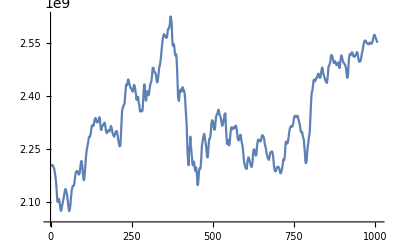

```mathematica
ListLinePlot[twapsWethUsdc90dFiltered1Week, PlotRange->All]
```

```mathematica
twapsWethUsdc90dFiltered2Week = Table[twapsWethUsdc90dFiltered[[i]], {i, 1, 2*6*24*7}]
```

{2.20799×10^9,2.20533×10^9,2.20572×10^9,2.20558×10^9,2.20476×10^9,2.2039×10^9,2.20513×10^9,2.2031×10^9,2.1997×10^9,2.1977×10^9,2.19642×10^9,2.19264×10^9,2.18452×10^9,2.17974×10^9,2.17409×10^9,2.16595×10^9,2.15763×10^9,2.14687×10^9,2.13229×10^9,2.11795×10^9,2.10658×10^9,2.10155×10^9,2.10459×10^9,2.10836×10^9,2.11006×10^9,2.10998×10^9,2.10671×10^9,2.09959×10^9,2.09156×10^9,2.08485×10^9,2.07922×10^9,2.07646×10^9,2.07685×10^9,2.08201×10^9,2.08605×10^9,2.0936×10^9,2.09635×10^9,2.10078×10^9,2.1063×10^9,2.11173×10^9,2.11541×10^9,2.12081×10^9,2.12707×10^9,2.13185×10^9,2.13614×10^9,2.13829×10^9,2.1356×10^9,2.13202×10^9,2.12948×10^9,2.12444×10^9,2.12109×10^9,2.11405×10^9,2.10656×10^9,2.09709×10^9,2.08876×10^9,2.08203×10^9,2.07571×10^9,2.076×10^9,2.07804×10^9,2.0826×10^9,2.092×10^9,2.10137×10^9,2.11342×10^9,2.12133×10^9,2.133×10^9,2.13803×10^9,2.14019×10^9,2.14584×10^9,2.14715×10^9,2.14686×10^9,2.14686×10^9,2.14853×10^9,2.15282×10^9,2.15936×10^9,2.16644×10^9,2.17366×10^9,2.18035×10^9,2.18508×10^9,2.18679×10^9,2.18661×10^9,2.18817×10^9,2.18892×10^9,2.18838×10^9,2.18555×10^9,2.18398×10^9,2.18084×10^9,2.17902×10^9,2.1791×10^9,2.18103×10^9,2.18514×10^9,2.19238×10^9,2.1997×10^9,2.20797×10^9,2.21494×10^9,2.21708×10^9,2.21531×10^9,2.20923×10^9,2.20054×10^9,2.19002×10^9,2.1798×10^9,2.17015×10^9,2.16504×10^9,2.16313×10^9,2.16575×10^9,2.17722×10^9,2.18669×10^9,2.20064×10^9,2.21318×10^9,2.2252×10^9,2.23608×10^9,2.24299×10^9,2.25221×10^9,2.25492×10^9,2.25937×10^9,2.2656×10^9,2.26918×10^9,2.27751×10^9,2.28222×10^9,2.28527×10^9,2.28614×10^9,2.28598×10^9,2.28635×10^9,2.29055×10^9,2.29529×10^9,2.30221×10^9,2.30863×10^9,2.31448×10^9,2.31796×10^9,2.31814×10^9,2.31637×10^9,2.31586×10^9,2.3173×10^9,2.31787×10^9,2.32308×10^9,2.32914×10^9,2.33406×10^9,2.33557×10^9,2.3385×10^9,2.33849×10^9,2.33491×10^9,2.33032×10^9,2.32851×10^9,2.32627×10^9,2.32693×10^9,2.327×10^9,2.32861×10^9,2.32872×10^9,2.3323×10^9,2.33609×10^9,2.34017×10^9,2.34079×10^9,2.33792×10^9,2.32664×10^9,2.31713×10^9,2.30791×10^9,2.30481×10^9,2.30593×10^9,2.31122×10^9,2.31633×10^9,2.31671×10^9,2.31654×10^9,2.31869×10^9,2.31917×10^9,2.32151×10^9,2.32353×10^9,2.32558×10^9,2.32512×10^9,2.32216×10^9,2.31566×10^9,2.30797×10^9,2.30158×10^9,2.30019×10^9,2.29582×10^9,2.29745×10^9,2.29969×10^9,2.3025×10^9,2.30329×10^9,2.30422×10^9,2.30287×10^9,2.3013×10^9,2.30039×10^9,2.30185×10^9,2.30393×10^9,2.30631×10^9,2.31256×10^9,2.31628×10^9,2.31432×10^9,2.31156×10^9,2.30752×10^9,2.30176×10^9,2.29729×10^9,2.29414×10^9,2.2911×10^9,2.28937×10^9,2.28748×10^9,2.28608×10^9,2.2887×10^9,2.29112×10^9,2.29267×10^9,2.29639×10^9,2.29873×10^9,2.30062×10^9,2.30202×10^9,2.3014×10^9,2.29931×10^9,2.29393×10^9,2.28801×10^9,2.28086×10^9,2.27559×10^9,2.27101×10^9,2.26585×10^9,2.26218×10^9,2.25884×10^9,2.25879×10^9,2.26032×10^9,2.27399×10^9,2.28924×10^9,2.31057×10^9,2.32906×10^9,2.35018×10^9,2.35935×10^9,2.36454×10^9,2.36951×10^9,2.37057×10^9,2.37302×10^9,2.37608×10^9,2.37666×10^9,2.37942×10^9,2.38804×10^9,2.3999×10^9,2.41264×10^9,2.42281×10^9,2.43272×10^9,2.43379×10^9,2.43288×10^9,2.43142×10^9,2.43641×10^9,2.44261×10^9,2.44738×10^9,2.44744×10^9,2.44522×10^9,2.43939×10^9,2.43497×10^9,2.43264×10^9,2.42861×10^9,2.42458×10^9,2.42349×10^9,2.42339×10^9,2.42106×10^9,2.41978×10^9,2.41792×10^9,2.41518×10^9,2.41306×10^9,2.41496×10^9,2.42005×10^9,2.42622×10^9,2.43092×10^9,2.43237×10^9,2.43004×10^9,2.42582×10^9,2.42046×10^9,2.41259×10^9,2.40775×10^9,2.40375×10^9,2.39108×10^9,2.39655×10^9,2.3956×10^9,2.39224×10^9,2.38944×10^9,2.39842×10^9,2.38836×10^9,2.38184×10^9,2.3781×10^9,2.3728×10^9,2.36321×10^9,2.35704×10^9,2.35824×10^9,2.36068×10^9,2.3603×10^9,2.36015×10^9,2.3579×10^9,2.35752×10^9,2.35909×10^9,2.36502×10^9,2.37908×10^9,2.39834×10^9,2.4127×10^9,2.42598×10^9,2.43401×10^9,2.43222×10^9,2.41886×10^9,2.40246×10^9,2.39316×10^9,2.38761×10^9,2.38868×10^9,2.40099×10^9,2.41134×10^9,2.41463×10^9,2.41221×10^9,2.40891×10^9,2.40558×10^9,2.40312×10^9,2.40413×10^9,2.41017×10^9,2.41718×10^9,2.4245×10^9,2.43149×10^9,2.43396×10^9,2.43713×10^9,2.43943×10^9,2.44341×10^9,2.45213×10^9,2.45836×10^9,2.47155×10^9,2.47967×10^9,2.48092×10^9,2.48045×10^9,2.47832×10^9,2.47252×10^9,2.46923×10^9,2.46871×10^9,2.46728×10^9,2.46567×10^9,2.46427×10^9,2.45963×10^9,2.45423×10^9,2.44689×10^9,2.44154×10^9,2.43926×10^9,2.44175×10^9,2.44538×10^9,2.45511×10^9,2.46241×10^9,2.47271×10^9,2.47959×10^9,2.48489×10^9,2.48836×10^9,2.49389×10^9,2.49936×10^9,2.50627×10^9,2.51533×10^9,2.52654×10^9,2.53708×10^9,2.54547×10^9,2.55359×10^9,2.56074×10^9,2.5665×10^9,2.57023×10^9,2.57431×10^9,2.57599×10^9,2.57284×10^9,2.57025×10^9,2.56978×10^9,2.56996×10^9,2.56804×10^9,2.56612×10^9,2.56696×10^9,2.56592×10^9,2.56733×10^9,2.57437×10^9,2.58211×10^9,2.58779×10^9,2.59054×10^9,2.59214×10^9,2.59185×10^9,2.59371×10^9,2.59943×10^9,2.60624×10^9,2.61565×10^9,2.6257×10^9,2.62317×10^9,2.61751×10^9,2.60893×10^9,2.59826×10^9,2.56573×10^9,2.55281×10^9,2.54389×10^9,2.54209×10^9,2.54473×10^9,2.54821×10^9,2.54514×10^9,2.53653×10^9,2.52562×10^9,2.51813×10^9,2.5154×10^9,2.51558×10^9,2.51916×10^9,2.51323×10^9,2.49936×10^9,2.48124×10^9,2.45851×10^9,2.42959×10^9,2.40366×10^9,2.39405×10^9,2.38788×10^9,2.38704×10^9,2.39695×10^9,2.41192×10^9,2.41702×10^9,2.41739×10^9,2.4192×10^9,2.41777×10^9,2.4136×10^9,2.41326×10^9,2.4183×10^9,2.42198×10^9,2.42571×10^9,2.42369×10^9,2.41881×10^9,2.41632×10^9,2.417×10^9,2.41421×10^9,2.41041×10^9,2.40525×10^9,2.39325×10^9,2.3742×10^9,2.35997×10^9,2.34364×10^9,2.33289×10^9,2.31322×10^9,2.28152×10^9,2.25267×10^9,2.2342×10^9,2.21876×10^9,2.21877×10^9,2.20542×10^9,2.24012×10^9,2.25011×10^9,2.25639×10^9,2.26274×10^9,2.28594×10^9,2.25998×10^9,2.25792×10^9,2.24987×10^9,2.23585×10^9,2.23095×10^9,2.21622×10^9,2.20627×10^9,2.20518×10^9,2.20774×10^9,2.20858×10^9,2.21536×10^9,2.21222×10^9,2.201×10^9,2.19372×10^9,2.18937×10^9,2.1898×10^9,2.19679×10^9,2.19911×10^9,2.1922×10^9,2.1814×10^9,2.16775×10^9,2.15329×10^9,2.14905×10^9,2.15453×10^9,2.16311×10^9,2.17754×10^9,2.1886×10^9,2.19496×10^9,2.19521×10^9,2.19642×10^9,2.19586×10^9,2.20198×10^9,2.21422×10^9,2.22915×10^9,2.24864×10^9,2.26186×10^9,2.26818×10^9,2.27401×10^9,2.27947×10^9,2.28488×10^9,2.28763×10^9,2.29374×10^9,2.2935×10^9,2.28949×10^9,2.28122×10^9,2.27718×10^9,2.26861×10^9,2.26267×10^9,2.25558×10^9,2.24668×10^9,2.23444×10^9,2.22963×10^9,2.22708×10^9,2.23103×10^9,2.2414×10^9,2.25694×10^9,2.26796×10^9,2.27638×10^9,2.28157×10^9,2.28064×10^9,2.28194×10^9,2.28855×10^9,2.29747×10^9,2.30827×10^9,2.32178×10^9,2.32668×10^9,2.33208×10^9,2.33238×10^9,2.3302×10^9,2.32706×10^9,2.32483×10^9,2.31294×10^9,2.30725×10^9,2.30586×10^9,2.30549×10^9,2.30875×10^9,2.32069×10^9,2.3289×10^9,2.33887×10^9,2.34455×10^9,2.34705×10^9,2.34831×10^9,2.34906×10^9,2.35316×10^9,2.35714×10^9,2.35986×10^9,2.36222×10^9,2.3601×10^9,2.3539×10^9,2.34852×10^9,2.34723×10^9,2.34445×10^9,2.34153×10^9,2.33929×10^9,2.33339×10^9,2.32678×10^9,2.32081×10^9,2.31699×10^9,2.31726×10^9,2.32052×10^9,2.32377×10^9,2.32889×10^9,2.33394×10^9,2.33811×10^9,2.34591×10^9,2.35097×10^9,2.3484×10^9,2.35168×10^9,2.32961×10^9,2.31129×10^9,2.29316×10^9,2.28242×10^9,2.26549×10^9,2.27423×10^9,2.27616×10^9,2.27699×10^9,2.27214×10^9,2.26531×10^9,2.26117×10^9,2.26262×10^9,2.26374×10^9,2.27259×10^9,2.28756×10^9,2.29605×10^9,2.30558×10^9,2.31085×10^9,2.31211×10^9,2.30824×10^9,2.30791×10^9,2.30698×10^9,2.30738×10^9,2.30927×10^9,2.31281×10^9,2.31167×10^9,2.31119×10^9,2.31043×10^9,2.31036×10^9,2.31235×10^9,2.31484×10^9,2.31729×10^9,2.31702×10^9,2.31256×10^9,2.30616×10^9,2.30047×10^9,2.29057×10^9,2.28115×10^9,2.27844×10^9,2.27622×10^9,2.27517×10^9,2.27651×10^9,2.28024×10^9,2.2841×10^9,2.28743×10^9,2.29157×10^9,2.29036×10^9,2.28662×10^9,2.2796×10^9,2.27321×10^9,2.26679×10^9,2.26409×10^9,2.25823×10^9,2.25215×10^9,2.24222×10^9,2.2328×10^9,2.22194×10^9,2.21341×10^9,2.20809×10^9,2.20552×10^9,2.20414×10^9,2.19895×10^9,2.19647×10^9,2.19691×10^9,2.19647×10^9,2.19503×10^9,2.20427×10^9,2.21535×10^9,2.2193×10^9,2.22389×10^9,2.22751×10^9,2.22651×10^9,2.22377×10^9,2.22182×10^9,2.21675×10^9,2.21353×10^9,2.2085×10^9,2.2066×10^9,2.2045×10^9,2.20086×10^9,2.20024×10^9,2.20296×10^9,2.2091×10^9,2.21676×10^9,2.23307×10^9,2.24249×10^9,2.24753×10^9,2.25021×10^9,2.24966×10^9,2.24755×10^9,2.2456×10^9,2.23852×10^9,2.23414×10^9,2.2323×10^9,2.23331×10^9,2.23724×10^9,2.25193×10^9,2.26192×10^9,2.2681×10^9,2.27309×10^9,2.27821×10^9,2.27709×10^9,2.27605×10^9,2.2762×10^9,2.27657×10^9,2.2759×10^9,2.27331×10^9,2.27229×10^9,2.27357×10^9,2.27615×10^9,2.27991×10^9,2.28524×10^9,2.28907×10^9,2.28996×10^9,2.28935×10^9,2.28902×10^9,2.28737×10^9,2.28427×10^9,2.28126×10^9,2.27787×10^9,2.2695×10^9,2.2637×10^9,2.25955×10^9,2.25705×10^9,2.25289×10^9,2.24485×10^9,2.23883×10^9,2.23579×10^9,2.23314×10^9,2.22735×10^9,2.22636×10^9,2.22483×10^9,2.22245×10^9,2.2202×10^9,2.22366×10^9,2.22793×10^9,2.23311×10^9,2.23822×10^9,2.24126×10^9,2.2419×10^9,2.2428×10^9,2.2431×10^9,2.24391×10^9,2.24438×10^9,2.24251×10^9,2.23764×10^9,2.23285×10^9,2.22346×10^9,2.21278×10^9,2.20363×10^9,2.19764×10^9,2.19271×10^9,2.18978×10^9,2.18801×10^9,2.18846×10^9,2.18976×10^9,2.19189×10^9,2.19508×10^9,2.19872×10^9,2.19979×10^9,2.20061×10^9,2.20091×10^9,2.20067×10^9,2.20039×10^9,2.19911×10^9,2.19718×10^9,2.19265×10^9,2.18857×10^9,2.18462×10^9,2.18244×10^9,2.18365×10^9,2.18494×10^9,2.18744×10^9,2.19216×10^9,2.19477×10^9,2.20087×10^9,2.20936×10^9,2.21653×10^9,2.22071×10^9,2.2223×10^9,2.2192×10^9,2.22228×10^9,2.22865×10^9,2.23954×10^9,2.25415×10^9,2.26709×10^9,2.27141×10^9,2.27257×10^9,2.26885×10^9,2.26645×10^9,2.26725×10^9,2.26852×10^9,2.27247×10^9,2.27791×10^9,2.28419×10^9,2.29287×10^9,2.29906×10^9,2.30388×10^9,2.30929×10^9,2.31112×10^9,2.31317×10^9,2.31564×10^9,2.31573×10^9,2.31561×10^9,2.31542×10^9,2.31413×10^9,2.31519×10^9,2.31908×10^9,2.32147×10^9,2.32736×10^9,2.33494×10^9,2.33998×10^9,2.34386×10^9,2.34424×10^9,2.34487×10^9,2.34497×10^9,2.34218×10^9,2.34076×10^9,2.3418×10^9,2.34242×10^9,2.34246×10^9,2.34516×10^9,2.34479×10^9,2.34044×10^9,2.33679×10^9,2.33343×10^9,2.3292×10^9,2.32519×10^9,2.32298×10^9,2.31663×10^9,2.30992×10^9,2.3041×10^9,2.29961×10^9,2.29866×10^9,2.29799×10^9,2.29939×10^9,2.2985×10^9,2.29236×10^9,2.28655×10^9,2.28392×10^9,2.2809×10^9,2.27635×10^9,2.26595×10^9,2.25331×10^9,2.24366×10^9,2.22887×10^9,2.2145×10^9,2.21107×10^9,2.21254×10^9,2.21443×10^9,2.22275×10^9,2.23622×10^9,2.24861×10^9,2.2594×10^9,2.26408×10^9,2.27033×10^9,2.2803×10^9,2.28652×10^9,2.29094×10^9,2.2981×10^9,2.31555×10^9,2.3368×10^9,2.35786×10^9,2.3769×10^9,2.39538×10^9,2.40696×10^9,2.41176×10^9,2.41569×10^9,2.42174×10^9,2.42885×10^9,2.4366×10^9,2.44476×10^9,2.44712×10^9,2.44617×10^9,2.44403×10^9,2.44363×10^9,2.44219×10^9,2.44623×10^9,2.44958×10^9,2.45123×10^9,2.45112×10^9,2.45167×10^9,2.45407×10^9,2.45812×10^9,2.46162×10^9,2.46369×10^9,2.46427×10^9,2.46289×10^9,2.45751×10^9,2.45375×10^9,2.45255×10^9,2.4526×10^9,2.45302×10^9,2.45883×10^9,2.46523×10^9,2.47045×10^9,2.47648×10^9,2.48128×10^9,2.48101×10^9,2.47698×10^9,2.47104×10^9,2.46507×10^9,2.46046×10^9,2.45761×10^9,2.45548×10^9,2.45276×10^9,2.44984×10^9,2.44595×10^9,2.44291×10^9,2.44226×10^9,2.44154×10^9,2.43928×10^9,2.43783×10^9,2.44323×10^9,2.45125×10^9,2.45873×10^9,2.47179×10^9,2.48318×10^9,2.48587×10^9,2.48714×10^9,2.48866×10^9,2.49182×10^9,2.49573×10^9,2.50131×10^9,2.50888×10^9,2.51503×10^9,2.51715×10^9,2.51551×10^9,2.5143×10^9,2.51203×10^9,2.50693×10^9,2.50391×10^9,2.49954×10^9,2.49506×10^9,2.49414×10^9,2.49543×10^9,2.49693×10^9,2.4989×10^9,2.49877×10^9,2.49364×10^9,2.49147×10^9,2.48988×10^9,2.48811×10^9,2.48799×10^9,2.48933×10^9,2.49132×10^9,2.49484×10^9,2.49545×10^9,2.49487×10^9,2.48933×10^9,2.48526×10^9,2.48001×10^9,2.48286×10^9,2.49015×10^9,2.50192×10^9,2.50791×10^9,2.51492×10^9,2.51568×10^9,2.51417×10^9,2.50893×10^9,2.50468×10^9,2.50156×10^9,2.49831×10^9,2.49638×10^9,2.49477×10^9,2.49335×10^9,2.49183×10^9,2.49079×10^9,2.48908×10^9,2.48649×10^9,2.48389×10^9,2.48105×10^9,2.47142×10^9,2.46433×10^9,2.45583×10^9,2.45223×10^9,2.45422×10^9,2.46197×10^9,2.47306×10^9,2.4924×10^9,2.50467×10^9,2.51184×10^9,2.51584×10^9,2.51972×10^9,2.51729×10^9,2.51696×10^9,2.51681×10^9,2.51826×10^9,2.52155×10^9,2.52454×10^9,2.52341×10^9,2.52264×10^9,2.52008×10^9,2.51702×10^9,2.51238×10^9,2.51208×10^9,2.51191×10^9,2.51242×10^9,2.51245×10^9,2.5126×10^9,2.51481×10^9,2.51713×10^9,2.51884×10^9,2.52143×10^9,2.5239×10^9,2.52503×10^9,2.52365×10^9,2.51914×10^9,2.51419×10^9,2.50823×10^9,2.50277×10^9,2.49839×10^9,2.49751×10^9,2.49796×10^9,2.49829×10^9,2.49901×10^9,2.50106×10^9,2.50468×10^9,2.50984×10^9,2.51568×10^9,2.52184×10^9,2.52488×10^9,2.52826×10^9,2.53554×10^9,2.53955×10^9,2.54475×10^9,2.54931×10^9,2.55421×10^9,2.55606×10^9,2.55704×10^9,2.558×10^9,2.55742×10^9,2.55613×10^9,2.55383×10^9,2.55188×10^9,2.55033×10^9,2.55004×10^9,2.54953×10^9,2.54977×10^9,2.54832×10^9,2.54754×10^9,2.547×10^9,2.54779×10^9,2.54815×10^9,2.5505×10^9,2.55165×10^9,2.55143×10^9,2.55092×10^9,2.55027×10^9,2.54893×10^9,2.54858×10^9,2.55059×10^9,2.553×10^9,2.55592×10^9,2.55994×10^9,2.56424×10^9,2.56771×10^9,2.57182×10^9,2.57375×10^9,2.57396×10^9,2.57164×10^9,2.56896×10^9,2.56596×10^9,2.5636×10^9,2.56107×10^9,2.55891×10^9,2.5563×10^9,2.55368×10^9,2.55618×10^9,2.56814×10^9,2.57934×10^9,2.59744×10^9,2.61451×10^9,2.62719×10^9,2.63082×10^9,2.6356×10^9,2.64104×10^9,2.64795×10^9,2.65163×10^9,2.65855×10^9,2.65906×10^9,2.65748×10^9,2.65239×10^9,2.65007×10^9,2.64537×10^9,2.6422×10^9,2.63909×10^9,2.63922×10^9,2.63904×10^9,2.63858×10^9,2.63735×10^9,2.63764×10^9,2.63803×10^9,2.63722×10^9,2.63794×10^9,2.6394×10^9,2.63626×10^9,2.6309×10^9,2.62599×10^9,2.62427×10^9,2.62282×10^9,2.62459×10^9,2.62923×10^9,2.63363×10^9,2.63453×10^9,2.63619×10^9,2.63742×10^9,2.6365×10^9,2.63813×10^9,2.63956×10^9,2.63923×10^9,2.63813×10^9,2.63675×10^9,2.63277×10^9,2.62774×10^9,2.6252×10^9,2.62523×10^9,2.62802×10^9,2.63213×10^9,2.63998×10^9,2.65069×10^9,2.66276×10^9,2.67138×10^9,2.67884×10^9,2.6839×10^9,2.68591×10^9,2.68649×10^9,2.68838×10^9,2.69162×10^9,2.69579×10^9,2.69895×10^9,2.70219×10^9,2.70203×10^9,2.6985×10^9,2.69107×10^9,2.68116×10^9,2.6707×10^9,2.65959×10^9,2.65079×10^9,2.6437×10^9,2.64043×10^9,2.63928×10^9,2.63988×10^9,2.6411×10^9,2.64281×10^9,2.6419×10^9,2.63996×10^9,2.63913×10^9,2.63692×10^9,2.63059×10^9,2.629×10^9,2.62375×10^9,2.6125×10^9,2.6043×10^9,2.59472×10^9,2.59248×10^9,2.58477×10^9,2.58679×10^9,2.59057×10^9,2.5975×10^9,2.60157×10^9,2.60817×10^9,2.61214×10^9,2.61509×10^9,2.61697×10^9,2.61809×10^9,2.61915×10^9,2.61857×10^9,2.61463×10^9,2.60977×10^9,2.60421×10^9,2.6001×10^9,2.60019×10^9,2.60194×10^9,2.60676×10^9,2.61245×10^9,2.61714×10^9,2.62146×10^9,2.62891×10^9,2.63716×10^9,2.64614×10^9,2.65821×10^9,2.67367×10^9,2.68377×10^9,2.69346×10^9,2.70188×10^9,2.70791×10^9,2.71172×10^9,2.71441×10^9,2.71902×10^9,2.71242×10^9,2.70675×10^9,2.70174×10^9,2.69608×10^9,2.69353×10^9,2.69857×10^9,2.7032×10^9,2.70851×10^9,2.71255×10^9,2.71347×10^9,2.71033×10^9,2.70519×10^9,2.69555×10^9,2.68986×10^9,2.68374×10^9,2.68337×10^9,2.68503×10^9,2.68906×10^9,2.69365×10^9,2.70085×10^9,2.7055×10^9,2.71066×10^9,2.71477×10^9,2.71774×10^9,2.71978×10^9,2.71976×10^9,2.71957×10^9,2.72293×10^9,2.72605×10^9,2.72826×10^9,2.61748×10^9,2.72971×10^9,2.72785×10^9,2.72473×10^9,2.72449×10^9,2.83875×10^9,2.73048×10^9,2.70685×10^9,2.72574×10^9,2.72363×10^9,2.71831×10^9,2.71326×10^9,2.73625×10^9,2.71169×10^9,2.71164×10^9,2.71516×10^9,2.72376×10^9,2.73414×10^9,2.74182×10^9,2.74377×10^9,2.74286×10^9,2.73679×10^9,2.72737×10^9,2.72313×10^9,2.72223×10^9,2.72211×10^9,2.72412×10^9,2.73119×10^9,2.73578×10^9,2.73961×10^9,2.74275×10^9,2.74377×10^9,2.74148×10^9,2.73802×10^9,2.73215×10^9,2.72686×10^9,2.72274×10^9,2.71851×10^9,2.71589×10^9,2.71682×10^9,2.71852×10^9,2.71973×10^9,2.72099×10^9,2.72118×10^9,2.72036×10^9,2.71803×10^9,2.71711×10^9,2.71625×10^9,2.71402×10^9,2.7077×10^9,2.70253×10^9,2.69641×10^9,2.69104×10^9,2.68881×10^9,2.6873×10^9,2.68706×10^9,2.68928×10^9,2.69198×10^9,2.69406×10^9,2.69883×10^9,2.70389×10^9,2.70778×10^9,2.71183×10^9,2.71527×10^9,2.72096×10^9,2.72397×10^9,2.72755×10^9,2.72925×10^9,2.72992×10^9,2.73064×10^9,2.73154×10^9,2.73126×10^9,2.73096×10^9,2.7294×10^9,2.72633×10^9,2.724×10^9,2.72102×10^9,2.71824×10^9,2.72097×10^9,2.72841×10^9,2.73666×10^9,2.74697×10^9,2.75731×10^9,2.7641×10^9,2.76504×10^9,2.76546×10^9,2.76513×10^9,2.76459×10^9,2.76491×10^9,2.76668×10^9,2.76743×10^9,2.76769×10^9,2.76806×10^9,2.76717×10^9,2.76543×10^9,2.76721×10^9,2.77086×10^9,2.775×10^9,2.78064×10^9,2.78663×10^9,2.78752×10^9,2.78625×10^9,2.78341×10^9,2.77901×10^9,2.77219×10^9,2.76783×10^9,2.76488×10^9,2.76346×10^9,2.7638×10^9,2.76513×10^9,2.7666×10^9,2.76932×10^9,2.77417×10^9,2.77752×10^9,2.78108×10^9,2.7845×10^9,2.78344×10^9,2.77817×10^9,2.77243×10^9,2.76555×10^9,2.75762×10^9,2.74739×10^9,2.74127×10^9,2.738×10^9,2.7346×10^9,2.73519×10^9,2.73259×10^9,2.72757×10^9,2.72235×10^9,2.7184×10^9,2.71327×10^9,2.71615×10^9,2.71967×10^9,2.72248×10^9,2.72501×10^9,2.72742×10^9,2.72738×10^9,2.72296×10^9,2.71582×10^9,2.71306×10^9,2.71057×10^9,2.70641×10^9,2.70649×10^9,2.70927×10^9,2.7094×10^9,2.70879×10^9,2.71196×10^9,2.71795×10^9,2.72507×10^9,2.73315×10^9,2.74055×10^9,2.74832×10^9,2.7532×10^9,2.75747×10^9,2.76008×10^9,2.76143×10^9,2.76196×10^9,2.76191×10^9,2.76149×10^9,2.75977×10^9,2.7548×10^9,2.75368×10^9,2.75089×10^9,2.7477×10^9,2.74435×10^9,2.74318×10^9,2.73905×10^9,2.73823×10^9,2.73931×10^9,2.74195×10^9,2.74371×10^9,2.74567×10^9,2.74399×10^9,2.74219×10^9,2.7421×10^9,2.74112×10^9,2.74029×10^9,2.74087×10^9,2.74219×10^9,2.74109×10^9,2.7422×10^9,2.74414×10^9,2.74721×10^9,2.75003×10^9,2.75336×10^9,2.75674×10^9,2.75873×10^9,2.76045×10^9,2.76198×10^9,2.7632×10^9,2.76403×10^9,2.76461×10^9,2.76565×10^9,2.76728×10^9,2.77046×10^9,2.77379×10^9,2.77742×10^9,2.78123×10^9,2.78293×10^9,2.7827×10^9,2.78245×10^9,2.78097×10^9,2.77977×10^9,2.77746×10^9,2.77616×10^9,2.77466×10^9,2.77401×10^9,2.77533×10^9,2.7787×10^9,2.78216×10^9,2.80134×10^9,2.78906×10^9,2.78842×10^9,2.78723×10^9,2.82806×10^9,2.76798×10^9,2.78159×10^9,2.7813×10^9,2.77825×10^9,2.72922×10^9,2.76753×10^9,2.76317×10^9,2.75753×10^9,2.75353×10^9,2.75102×10^9,2.7483×10^9,2.74567×10^9,2.74392×10^9,2.74468×10^9,2.74638×10^9,2.74819×10^9,2.7477×10^9,2.74719×10^9,2.74595×10^9,2.74403×10^9,2.74128×10^9,2.74355×10^9,2.74612×10^9,2.7494×10^9,2.75331×10^9,2.75533×10^9,2.75248×10^9,2.7507×10^9,2.74822×10^9,2.74593×10^9,2.7459×10^9,2.74559×10^9,2.74579×10^9,2.74671×10^9,2.74729×10^9,2.7484×10^9,2.75239×10^9,2.75614×10^9,2.75919×10^9,2.76152×10^9,2.7637×10^9,2.76366×10^9,2.76471×10^9,2.76466×10^9,2.76468×10^9,2.76518×10^9,2.76498×10^9,2.76413×10^9,2.76529×10^9,2.76855×10^9,2.77194×10^9,2.77473×10^9,2.77689×10^9,2.77822×10^9,2.77799×10^9,2.77618×10^9,2.77409×10^9,2.77224×10^9,2.76982×10^9,2.76719×10^9,2.7649×10^9,2.7613×10^9,2.75929×10^9,2.75776×10^9,2.75645×10^9,2.75597×10^9,2.75652×10^9,2.75541×10^9,2.7544×10^9,2.75292×10^9,2.75267×10^9,2.75227×10^9,2.7536×10^9,2.75607×10^9,2.75943×10^9,2.76309×10^9,2.76715×10^9,2.76933×10^9,2.77048×10^9,2.77078×10^9,2.77071×10^9,2.76979×10^9,2.76909×10^9,2.76776×10^9,2.76768×10^9,2.76883×10^9,2.77949×10^9,2.79242×10^9,2.80527×10^9,2.81563×10^9,2.82967×10^9,2.83186×10^9,2.83186×10^9,2.83116×10^9,2.83322×10^9,2.83502×10^9,2.83731×10^9,2.8405×10^9,2.84328×10^9,2.84375×10^9,2.84361×10^9,2.84323×10^9,2.84274×10^9,2.84259×10^9,2.84563×10^9,2.85031×10^9,2.85527×10^9,2.85864×10^9,2.86233×10^9,2.86076×10^9,2.85856×10^9,2.85557×10^9,2.85439×10^9,2.85513×10^9,2.85625×10^9,2.85655×10^9,2.85682×10^9,2.85649×10^9,2.85557×10^9,2.85521×10^9,2.85615×10^9,2.85757×10^9,2.85818×10^9,2.8577×10^9,2.85372×10^9,2.84594×10^9,2.83934×10^9,2.83444×10^9,2.8325×10^9,2.83316×10^9,2.83598×10^9,2.8374×10^9,2.83687×10^9,2.83468×10^9,2.83461×10^9,2.83743×10^9,2.84098×10^9,2.84543×10^9,2.84947×10^9,2.8527×10^9,2.854×10^9,2.8552×10^9,2.85894×10^9,2.8634×10^9,2.86716×10^9,2.87105×10^9,2.87345×10^9,2.87385×10^9,2.87273×10^9,2.87143×10^9,2.86996×10^9,2.86907×10^9,2.86878×10^9,2.86857×10^9,2.86782×10^9,2.86742×10^9,2.86603×10^9,2.8637×10^9,2.86046×10^9,2.85818×10^9,2.85434×10^9,2.8527×10^9,2.85328×10^9,2.85804×10^9,2.86276×10^9,2.86969×10^9,2.87547×10^9,2.80645×10^9,2.88817×10^9,2.89516×10^9,2.90277×10^9,2.90995×10^9,2.99492×10^9,2.92215×10^9,2.92512×10^9,2.9281×10^9,2.93023×10^9,2.93112×10^9,2.9317×10^9,2.93274×10^9,2.93337×10^9,2.93337×10^9,2.93266×10^9,2.92963×10^9,2.92575×10^9,2.92503×10^9,2.92361×10^9,2.9247×10^9,2.9292×10^9,2.93421×10^9,2.93769×10^9,3.03478×10^9,2.93804×10^9,2.93441×10^9,2.93127×10^9,2.92849×10^9,2.84973×10^9,2.9289×10^9,2.93166×10^9,2.93378×10^9,2.93654×10^9,2.93757×10^9,2.93919×10^9,2.94188×10^9,2.94373×10^9,2.94649×10^9,2.94615×10^9,2.94533×10^9,2.94334×10^9,2.9416×10^9,2.93936×10^9,2.93819×10^9,2.93651×10^9,2.93576×10^9,2.93568×10^9,2.93596×10^9,2.93709×10^9,2.93933×10^9,2.94297×10^9,2.94542×10^9,2.94764×10^9,2.94994×10^9,2.95137×10^9,2.9515×10^9,2.95024×10^9,2.94409×10^9,2.93685×10^9,2.92533×10^9,2.91281×10^9,2.91113×10^9,2.91184×10^9,2.91191×10^9,2.91431×10^9,2.91738×10^9,2.91731×10^9,2.91522×10^9,2.91575×10^9,2.91633×10^9,2.9172×10^9,2.91769×10^9,2.91803×10^9,2.91747×10^9,2.91558×10^9,2.90994×10^9,2.90433×10^9,2.89991×10^9,2.89507×10^9,2.89195×10^9,2.88844×10^9,2.88498×10^9,2.87998×10^9,2.87532×10^9,2.87316×10^9,2.87376×10^9,2.875×10^9,2.87711×10^9,2.87898×10^9,2.88206×10^9,2.88564×10^9,2.89221×10^9,2.89905×10^9,2.90687×10^9,2.91168×10^9,2.9154×10^9,2.91581×10^9,2.91519×10^9,2.91474×10^9,2.91469×10^9,2.91541×10^9,2.91761×10^9,2.9211×10^9,2.92439×10^9,2.92719×10^9,2.92829×10^9,2.92738×10^9,2.92673×10^9,2.92583×10^9,2.92599×10^9,2.92453×10^9,2.92212×10^9,2.92077×10^9,2.91849×10^9,2.9166×10^9,2.9168×10^9,2.91798×10^9,2.91889×10^9,2.91928×10^9,2.91902×10^9,2.81586×10^9,2.91997×10^9,2.92207×10^9,2.92466×10^9,2.92757×10^9,3.04472×10^9,2.93313×10^9,2.93374×10^9,2.93474×10^9,2.93518×10^9,2.93494×10^9,2.93477×10^9,2.93473×10^9,2.93493×10^9,2.93632×10^9,2.938×10^9,2.94001×10^9,2.94144×10^9,2.94487×10^9,2.94892×10^9,2.95266×10^9,2.9592×10^9,2.96545×10^9,2.96951×10^9,2.97281×10^9,2.97447×10^9,2.97448×10^9,2.97352×10^9,2.97196×10^9,2.97037×10^9,2.96885×10^9,2.96757×10^9,2.96789×10^9,2.96959×10^9,2.97161×10^9,2.97374×10^9,2.97396×10^9,2.97038×10^9,2.96509×10^9,2.95729×10^9,2.94817×10^9,2.94357×10^9,2.94192×10^9,2.94294×10^9,2.94426×10^9,2.94644×10^9,2.95175×10^9,2.95794×10^9,2.96718×10^9,2.97438×10^9,2.98319×10^9,2.98637×10^9,2.98854×10^9,2.99013×10^9,2.99205×10^9,2.99826×10^9,3.00421×10^9,3.00858×10^9,3.01404×10^9,3.01764×10^9,3.01749×10^9,3.01875×10^9,3.02059×10^9,3.02486×10^9,3.02954×10^9,3.03463×10^9,3.03939×10^9,3.04473×10^9,3.04978×10^9,3.05285×10^9,3.0543×10^9,3.05471×10^9,3.0537×10^9,3.05238×10^9,3.05422×10^9,3.05571×10^9,3.06099×10^9,3.0702×10^9,3.08027×10^9,3.08642×10^9,3.08984×10^9,3.09292×10^9,3.09329×10^9,3.09247×10^9,3.09069×10^9,3.0893×10^9,3.09236×10^9,3.10229×10^9,3.11249×10^9,3.12166×10^9,3.13349×10^9,3.14192×10^9,3.14816×10^9,3.1563×10^9,3.16645×10^9,3.17416×10^9,3.17874×10^9,3.1755×10^9,3.17232×10^9,3.16874×10^9,3.16586×10^9,3.16861×10^9,3.16742×10^9,3.16414×10^9,3.1593×10^9,3.15435×10^9,3.14781×10^9,3.14722×10^9,3.14946×10^9,3.15466×10^9,3.15986×10^9,3.16539×10^9,3.16726×10^9,3.16749×10^9,3.16459×10^9,3.15916×10^9,3.1508×10^9,3.14581×10^9,3.14291×10^9,3.13797×10^9,3.13545×10^9,3.13475×10^9,3.12745×10^9,3.12068×10^9,3.11636×10^9,3.11706×10^9,3.11962×10^9,3.12807×10^9,3.14131×10^9,3.1519×10^9,3.15746×10^9,3.1652×10^9,3.17054×10^9,3.17034×10^9,3.17038×10^9,3.17194×10^9,3.17099×10^9,3.16982×10^9,3.17997×10^9,3.19805×10^9,3.21332×10^9,3.2328×10^9,3.25006×10^9,3.26408×10^9,3.26847×10^9,3.27346×10^9,3.28292×10^9,3.28874×10^9,3.29368×10^9,3.30162×10^9,3.30984×10^9,3.31551×10^9,3.31525×10^9,3.30975×10^9,3.30738×10^9,3.30371×10^9,3.29632×10^9,3.29271×10^9,3.2954×10^9,3.291×10^9,3.28432×10^9,3.28393×10^9,3.28365×10^9,3.28322×10^9,3.28341×10^9,3.28726×10^9,3.28674×10^9,3.29249×10^9,3.30197×10^9,3.32134×10^9,3.34054×10^9,3.35925×10^9,3.37253×10^9,3.38068×10^9,3.38782×10^9,3.39434×10^9,3.40513×10^9,3.41667×10^9,3.42637×10^9,3.51266×10^9,3.41029×10^9,3.39725×10^9,3.38664×10^9,3.35792×10^9,3.24986×10^9,3.32865×10^9,3.31206×10^9,3.29581×10^9,3.29777×10^9,3.30036×10^9,3.29862×10^9,3.28909×10^9,3.27985×10^9,3.27262×10^9,3.25998×10^9,3.24619×10^9,3.24303×10^9,3.24156×10^9,3.24031×10^9,3.24427×10^9,3.24642×10^9,3.24701×10^9,3.25556×10^9,3.26539×10^9,3.27686×10^9,3.29305×10^9,3.31134×10^9,3.32849×10^9,3.34022×10^9,3.35294×10^9,3.35822×10^9,3.36525×10^9,3.3693×10^9,3.37145×10^9,3.37457×10^9,3.37841×10^9,3.37754×10^9,3.37142×10^9,3.36896×10^9,3.36567×10^9,3.3615×10^9,3.35694×10^9,3.35295×10^9,3.34424×10^9,3.33067×10^9,3.32129×10^9,3.31551×10^9,3.30967×10^9,3.30488×10^9,3.31224×10^9,3.31948×10^9,3.33212×10^9,3.34441×10^9,3.35342×10^9,3.35429×10^9,3.35717×10^9,3.36256×10^9,3.36871×10^9,3.38226×10^9,3.39839×10^9,3.40725×10^9,3.41138×10^9,3.41839×10^9,3.42868×10^9,3.43749×10^9,3.44802×10^9,3.45623×10^9,3.45604×10^9,3.45006×10^9,3.45079×10^9,3.44972×10^9,3.45783×10^9,3.46868×10^9,3.51917×10^9,3.49037×10^9,3.48956×10^9,3.49155×10^9,3.48313×10^9,3.4358×10^9,3.43892×10^9,3.42236×10^9,3.39615×10^9,3.37087×10^9,3.34657×10^9,3.31593×10^9,3.29004×10^9,3.28075×10^9,3.27893×10^9,3.2681×10^9,3.25206×10^9,3.25651×10^9,3.26333×10^9,3.266×10^9,3.27289×10^9,3.29005×10^9,3.30333×10^9,3.30959×10^9,3.31795×10^9,3.3263×10^9,3.33685×10^9,3.34964×10^9,3.35788×10^9,3.36501×10^9,3.37315×10^9,3.38492×10^9,3.38066×10^9,3.3892×10^9,3.40191×10^9,3.40186×10^9,3.38829×10^9,3.39475×10^9,3.38859×10^9,3.38107×10^9,3.38142×10^9,3.38023×10^9,3.37093×10^9,3.36058×10^9,3.35022×10^9,3.33532×10^9,3.31576×10^9,3.30652×10^9,3.28881×10^9,3.28516×10^9,3.28866×10^9,3.29359×10^9,3.29752×10^9,3.29343×10^9,3.28286×10^9,3.2772×10^9,3.27467×10^9,3.27531×10^9,3.28842×10^9,3.30126×10^9,3.31071×10^9,3.3224×10^9,3.33405×10^9,3.34239×10^9,3.35175×10^9,3.36104×10^9,3.36×10^9,3.3598×10^9,3.35398×10^9,3.34512×10^9,3.33837×10^9,3.32631×10^9,3.31173×10^9,3.30417×10^9,3.29825×10^9,3.29722×10^9,3.29596×10^9,3.29762×10^9,3.3007×10^9,3.30004×10^9,3.29202×10^9,3.28085×10^9,3.27257×10^9,3.26674×10^9,3.26707×10^9,3.2698×10^9,3.27276×10^9,3.27289×10^9,3.26668×10^9,3.25799×10^9,3.25262×10^9,3.25011×10^9,3.25127×10^9,3.25661×10^9,3.26576×10^9,3.27656×10^9,3.29321×10^9,3.31361×10^9,3.32532×10^9,3.3378×10^9,3.34953×10^9}

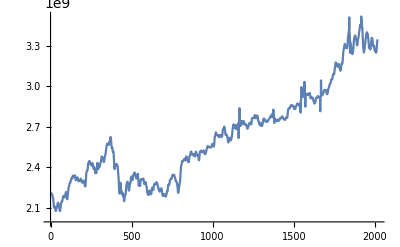

```mathematica
ListLinePlot[twapsWethUsdc90dFiltered2Week , PlotRange->All]
```

```mathematica
twapsWethUsdc90dFiltered2Week = Table[twapsWethUsdc90dFiltered[[i]], {i, 1, 2*6*24*7}]
```

{2.20799×10^9,2.20533×10^9,2.20572×10^9,2.20558×10^9,2.20476×10^9,2.2039×10^9,2.20513×10^9,2.2031×10^9,2.1997×10^9,2.1977×10^9,2.19642×10^9,2.19264×10^9,2.18452×10^9,2.17974×10^9,2.17409×10^9,2.16595×10^9,2.15763×10^9,2.14687×10^9,2.13229×10^9,2.11795×10^9,2.10658×10^9,2.10155×10^9,2.10459×10^9,2.10836×10^9,2.11006×10^9,2.10998×10^9,2.10671×10^9,2.09959×10^9,2.09156×10^9,2.08485×10^9,2.07922×10^9,2.07646×10^9,2.07685×10^9,2.08201×10^9,2.08605×10^9,2.0936×10^9,2.09635×10^9,2.10078×10^9,2.1063×10^9,2.11173×10^9,2.11541×10^9,2.12081×10^9,2.12707×10^9,2.13185×10^9,2.13614×10^9,2.13829×10^9,2.1356×10^9,2.13202×10^9,2.12948×10^9,2.12444×10^9,2.12109×10^9,2.11405×10^9,2.10656×10^9,2.09709×10^9,2.08876×10^9,2.08203×10^9,2.07571×10^9,2.076×10^9,2.07804×10^9,2.0826×10^9,2.092×10^9,2.10137×10^9,2.11342×10^9,2.12133×10^9,2.133×10^9,2.13803×10^9,2.14019×10^9,2.14584×10^9,2.14715×10^9,2.14686×10^9,2.14686×10^9,2.14853×10^9,2.15282×10^9,2.15936×10^9,2.16644×10^9,2.17366×10^9,2.18035×10^9,2.18508×10^9,2.18679×10^9,2.18661×10^9,2.18817×10^9,2.18892×10^9,2.18838×10^9,2.18555×10^9,2.18398×10^9,2.18084×10^9,2.17902×10^9,2.1791×10^9,2.18103×10^9,2.18514×10^9,2.19238×10^9,2.1997×10^9,2.20797×10^9,2.21494×10^9,2.21708×10^9,2.21531×10^9,2.20923×10^9,2.20054×10^9,2.19002×10^9,2.1798×10^9,2.17015×10^9,2.16504×10^9,2.16313×10^9,2.16575×10^9,2.17722×10^9,2.18669×10^9,2.20064×10^9,2.21318×10^9,2.2252×10^9,2.23608×10^9,2.24299×10^9,2.25221×10^9,2.25492×10^9,2.25937×10^9,2.2656×10^9,2.26918×10^9,2.27751×10^9,2.28222×10^9,2.28527×10^9,2.28614×10^9,2.28598×10^9,2.28635×10^9,2.29055×10^9,2.29529×10^9,2.30221×10^9,2.30863×10^9,2.31448×10^9,2.31796×10^9,2.31814×10^9,2.31637×10^9,2.31586×10^9,2.3173×10^9,2.31787×10^9,2.32308×10^9,2.32914×10^9,2.33406×10^9,2.33557×10^9,2.3385×10^9,2.33849×10^9,2.33491×10^9,2.33032×10^9,2.32851×10^9,2.32627×10^9,2.32693×10^9,2.327×10^9,2.32861×10^9,2.32872×10^9,2.3323×10^9,2.33609×10^9,2.34017×10^9,2.34079×10^9,2.33792×10^9,2.32664×10^9,2.31713×10^9,2.30791×10^9,2.30481×10^9,2.30593×10^9,2.31122×10^9,2.31633×10^9,2.31671×10^9,2.31654×10^9,2.31869×10^9,2.31917×10^9,2.32151×10^9,2.32353×10^9,2.32558×10^9,2.32512×10^9,2.32216×10^9,2.31566×10^9,2.30797×10^9,2.30158×10^9,2.30019×10^9,2.29582×10^9,2.29745×10^9,2.29969×10^9,2.3025×10^9,2.30329×10^9,2.30422×10^9,2.30287×10^9,2.3013×10^9,2.30039×10^9,2.30185×10^9,2.30393×10^9,2.30631×10^9,2.31256×10^9,2.31628×10^9,2.31432×10^9,2.31156×10^9,2.30752×10^9,2.30176×10^9,2.29729×10^9,2.29414×10^9,2.2911×10^9,2.28937×10^9,2.28748×10^9,2.28608×10^9,2.2887×10^9,2.29112×10^9,2.29267×10^9,2.29639×10^9,2.29873×10^9,2.30062×10^9,2.30202×10^9,2.3014×10^9,2.29931×10^9,2.29393×10^9,2.28801×10^9,2.28086×10^9,2.27559×10^9,2.27101×10^9,2.26585×10^9,2.26218×10^9,2.25884×10^9,2.25879×10^9,2.26032×10^9,2.27399×10^9,2.28924×10^9,2.31057×10^9,2.32906×10^9,2.35018×10^9,2.35935×10^9,2.36454×10^9,2.36951×10^9,2.37057×10^9,2.37302×10^9,2.37608×10^9,2.37666×10^9,2.37942×10^9,2.38804×10^9,2.3999×10^9,2.41264×10^9,2.42281×10^9,2.43272×10^9,2.43379×10^9,2.43288×10^9,2.43142×10^9,2.43641×10^9,2.44261×10^9,2.44738×10^9,2.44744×10^9,2.44522×10^9,2.43939×10^9,2.43497×10^9,2.43264×10^9,2.42861×10^9,2.42458×10^9,2.42349×10^9,2.42339×10^9,2.42106×10^9,2.41978×10^9,2.41792×10^9,2.41518×10^9,2.41306×10^9,2.41496×10^9,2.42005×10^9,2.42622×10^9,2.43092×10^9,2.43237×10^9,2.43004×10^9,2.42582×10^9,2.42046×10^9,2.41259×10^9,2.40775×10^9,2.40375×10^9,2.39108×10^9,2.39655×10^9,2.3956×10^9,2.39224×10^9,2.38944×10^9,2.39842×10^9,2.38836×10^9,2.38184×10^9,2.3781×10^9,2.3728×10^9,2.36321×10^9,2.35704×10^9,2.35824×10^9,2.36068×10^9,2.3603×10^9,2.36015×10^9,2.3579×10^9,2.35752×10^9,2.35909×10^9,2.36502×10^9,2.37908×10^9,2.39834×10^9,2.4127×10^9,2.42598×10^9,2.43401×10^9,2.43222×10^9,2.41886×10^9,2.40246×10^9,2.39316×10^9,2.38761×10^9,2.38868×10^9,2.40099×10^9,2.41134×10^9,2.41463×10^9,2.41221×10^9,2.40891×10^9,2.40558×10^9,2.40312×10^9,2.40413×10^9,2.41017×10^9,2.41718×10^9,2.4245×10^9,2.43149×10^9,2.43396×10^9,2.43713×10^9,2.43943×10^9,2.44341×10^9,2.45213×10^9,2.45836×10^9,2.47155×10^9,2.47967×10^9,2.48092×10^9,2.48045×10^9,2.47832×10^9,2.47252×10^9,2.46923×10^9,2.46871×10^9,2.46728×10^9,2.46567×10^9,2.46427×10^9,2.45963×10^9,2.45423×10^9,2.44689×10^9,2.44154×10^9,2.43926×10^9,2.44175×10^9,2.44538×10^9,2.45511×10^9,2.46241×10^9,2.47271×10^9,2.47959×10^9,2.48489×10^9,2.48836×10^9,2.49389×10^9,2.49936×10^9,2.50627×10^9,2.51533×10^9,2.52654×10^9,2.53708×10^9,2.54547×10^9,2.55359×10^9,2.56074×10^9,2.5665×10^9,2.57023×10^9,2.57431×10^9,2.57599×10^9,2.57284×10^9,2.57025×10^9,2.56978×10^9,2.56996×10^9,2.56804×10^9,2.56612×10^9,2.56696×10^9,2.56592×10^9,2.56733×10^9,2.57437×10^9,2.58211×10^9,2.58779×10^9,2.59054×10^9,2.59214×10^9,2.59185×10^9,2.59371×10^9,2.59943×10^9,2.60624×10^9,2.61565×10^9,2.6257×10^9,2.62317×10^9,2.61751×10^9,2.60893×10^9,2.59826×10^9,2.56573×10^9,2.55281×10^9,2.54389×10^9,2.54209×10^9,2.54473×10^9,2.54821×10^9,2.54514×10^9,2.53653×10^9,2.52562×10^9,2.51813×10^9,2.5154×10^9,2.51558×10^9,2.51916×10^9,2.51323×10^9,2.49936×10^9,2.48124×10^9,2.45851×10^9,2.42959×10^9,2.40366×10^9,2.39405×10^9,2.38788×10^9,2.38704×10^9,2.39695×10^9,2.41192×10^9,2.41702×10^9,2.41739×10^9,2.4192×10^9,2.41777×10^9,2.4136×10^9,2.41326×10^9,2.4183×10^9,2.42198×10^9,2.42571×10^9,2.42369×10^9,2.41881×10^9,2.41632×10^9,2.417×10^9,2.41421×10^9,2.41041×10^9,2.40525×10^9,2.39325×10^9,2.3742×10^9,2.35997×10^9,2.34364×10^9,2.33289×10^9,2.31322×10^9,2.28152×10^9,2.25267×10^9,2.2342×10^9,2.21876×10^9,2.21877×10^9,2.20542×10^9,2.24012×10^9,2.25011×10^9,2.25639×10^9,2.26274×10^9,2.28594×10^9,2.25998×10^9,2.25792×10^9,2.24987×10^9,2.23585×10^9,2.23095×10^9,2.21622×10^9,2.20627×10^9,2.20518×10^9,2.20774×10^9,2.20858×10^9,2.21536×10^9,2.21222×10^9,2.201×10^9,2.19372×10^9,2.18937×10^9,2.1898×10^9,2.19679×10^9,2.19911×10^9,2.1922×10^9,2.1814×10^9,2.16775×10^9,2.15329×10^9,2.14905×10^9,2.15453×10^9,2.16311×10^9,2.17754×10^9,2.1886×10^9,2.19496×10^9,2.19521×10^9,2.19642×10^9,2.19586×10^9,2.20198×10^9,2.21422×10^9,2.22915×10^9,2.24864×10^9,2.26186×10^9,2.26818×10^9,2.27401×10^9,2.27947×10^9,2.28488×10^9,2.28763×10^9,2.29374×10^9,2.2935×10^9,2.28949×10^9,2.28122×10^9,2.27718×10^9,2.26861×10^9,2.26267×10^9,2.25558×10^9,2.24668×10^9,2.23444×10^9,2.22963×10^9,2.22708×10^9,2.23103×10^9,2.2414×10^9,2.25694×10^9,2.26796×10^9,2.27638×10^9,2.28157×10^9,2.28064×10^9,2.28194×10^9,2.28855×10^9,2.29747×10^9,2.30827×10^9,2.32178×10^9,2.32668×10^9,2.33208×10^9,2.33238×10^9,2.3302×10^9,2.32706×10^9,2.32483×10^9,2.31294×10^9,2.30725×10^9,2.30586×10^9,2.30549×10^9,2.30875×10^9,2.32069×10^9,2.3289×10^9,2.33887×10^9,2.34455×10^9,2.34705×10^9,2.34831×10^9,2.34906×10^9,2.35316×10^9,2.35714×10^9,2.35986×10^9,2.36222×10^9,2.3601×10^9,2.3539×10^9,2.34852×10^9,2.34723×10^9,2.34445×10^9,2.34153×10^9,2.33929×10^9,2.33339×10^9,2.32678×10^9,2.32081×10^9,2.31699×10^9,2.31726×10^9,2.32052×10^9,2.32377×10^9,2.32889×10^9,2.33394×10^9,2.33811×10^9,2.34591×10^9,2.35097×10^9,2.3484×10^9,2.35168×10^9,2.32961×10^9,2.31129×10^9,2.29316×10^9,2.28242×10^9,2.26549×10^9,2.27423×10^9,2.27616×10^9,2.27699×10^9,2.27214×10^9,2.26531×10^9,2.26117×10^9,2.26262×10^9,2.26374×10^9,2.27259×10^9,2.28756×10^9,2.29605×10^9,2.30558×10^9,2.31085×10^9,2.31211×10^9,2.30824×10^9,2.30791×10^9,2.30698×10^9,2.30738×10^9,2.30927×10^9,2.31281×10^9,2.31167×10^9,2.31119×10^9,2.31043×10^9,2.31036×10^9,2.31235×10^9,2.31484×10^9,2.31729×10^9,2.31702×10^9,2.31256×10^9,2.30616×10^9,2.30047×10^9,2.29057×10^9,2.28115×10^9,2.27844×10^9,2.27622×10^9,2.27517×10^9,2.27651×10^9,2.28024×10^9,2.2841×10^9,2.28743×10^9,2.29157×10^9,2.29036×10^9,2.28662×10^9,2.2796×10^9,2.27321×10^9,2.26679×10^9,2.26409×10^9,2.25823×10^9,2.25215×10^9,2.24222×10^9,2.2328×10^9,2.22194×10^9,2.21341×10^9,2.20809×10^9,2.20552×10^9,2.20414×10^9,2.19895×10^9,2.19647×10^9,2.19691×10^9,2.19647×10^9,2.19503×10^9,2.20427×10^9,2.21535×10^9,2.2193×10^9,2.22389×10^9,2.22751×10^9,2.22651×10^9,2.22377×10^9,2.22182×10^9,2.21675×10^9,2.21353×10^9,2.2085×10^9,2.2066×10^9,2.2045×10^9,2.20086×10^9,2.20024×10^9,2.20296×10^9,2.2091×10^9,2.21676×10^9,2.23307×10^9,2.24249×10^9,2.24753×10^9,2.25021×10^9,2.24966×10^9,2.24755×10^9,2.2456×10^9,2.23852×10^9,2.23414×10^9,2.2323×10^9,2.23331×10^9,2.23724×10^9,2.25193×10^9,2.26192×10^9,2.2681×10^9,2.27309×10^9,2.27821×10^9,2.27709×10^9,2.27605×10^9,2.2762×10^9,2.27657×10^9,2.2759×10^9,2.27331×10^9,2.27229×10^9,2.27357×10^9,2.27615×10^9,2.27991×10^9,2.28524×10^9,2.28907×10^9,2.28996×10^9,2.28935×10^9,2.28902×10^9,2.28737×10^9,2.28427×10^9,2.28126×10^9,2.27787×10^9,2.2695×10^9,2.2637×10^9,2.25955×10^9,2.25705×10^9,2.25289×10^9,2.24485×10^9,2.23883×10^9,2.23579×10^9,2.23314×10^9,2.22735×10^9,2.22636×10^9,2.22483×10^9,2.22245×10^9,2.2202×10^9,2.22366×10^9,2.22793×10^9,2.23311×10^9,2.23822×10^9,2.24126×10^9,2.2419×10^9,2.2428×10^9,2.2431×10^9,2.24391×10^9,2.24438×10^9,2.24251×10^9,2.23764×10^9,2.23285×10^9,2.22346×10^9,2.21278×10^9,2.20363×10^9,2.19764×10^9,2.19271×10^9,2.18978×10^9,2.18801×10^9,2.18846×10^9,2.18976×10^9,2.19189×10^9,2.19508×10^9,2.19872×10^9,2.19979×10^9,2.20061×10^9,2.20091×10^9,2.20067×10^9,2.20039×10^9,2.19911×10^9,2.19718×10^9,2.19265×10^9,2.18857×10^9,2.18462×10^9,2.18244×10^9,2.18365×10^9,2.18494×10^9,2.18744×10^9,2.19216×10^9,2.19477×10^9,2.20087×10^9,2.20936×10^9,2.21653×10^9,2.22071×10^9,2.2223×10^9,2.2192×10^9,2.22228×10^9,2.22865×10^9,2.23954×10^9,2.25415×10^9,2.26709×10^9,2.27141×10^9,2.27257×10^9,2.26885×10^9,2.26645×10^9,2.26725×10^9,2.26852×10^9,2.27247×10^9,2.27791×10^9,2.28419×10^9,2.29287×10^9,2.29906×10^9,2.30388×10^9,2.30929×10^9,2.31112×10^9,2.31317×10^9,2.31564×10^9,2.31573×10^9,2.31561×10^9,2.31542×10^9,2.31413×10^9,2.31519×10^9,2.31908×10^9,2.32147×10^9,2.32736×10^9,2.33494×10^9,2.33998×10^9,2.34386×10^9,2.34424×10^9,2.34487×10^9,2.34497×10^9,2.34218×10^9,2.34076×10^9,2.3418×10^9,2.34242×10^9,2.34246×10^9,2.34516×10^9,2.34479×10^9,2.34044×10^9,2.33679×10^9,2.33343×10^9,2.3292×10^9,2.32519×10^9,2.32298×10^9,2.31663×10^9,2.30992×10^9,2.3041×10^9,2.29961×10^9,2.29866×10^9,2.29799×10^9,2.29939×10^9,2.2985×10^9,2.29236×10^9,2.28655×10^9,2.28392×10^9,2.2809×10^9,2.27635×10^9,2.26595×10^9,2.25331×10^9,2.24366×10^9,2.22887×10^9,2.2145×10^9,2.21107×10^9,2.21254×10^9,2.21443×10^9,2.22275×10^9,2.23622×10^9,2.24861×10^9,2.2594×10^9,2.26408×10^9,2.27033×10^9,2.2803×10^9,2.28652×10^9,2.29094×10^9,2.2981×10^9,2.31555×10^9,2.3368×10^9,2.35786×10^9,2.3769×10^9,2.39538×10^9,2.40696×10^9,2.41176×10^9,2.41569×10^9,2.42174×10^9,2.42885×10^9,2.4366×10^9,2.44476×10^9,2.44712×10^9,2.44617×10^9,2.44403×10^9,2.44363×10^9,2.44219×10^9,2.44623×10^9,2.44958×10^9,2.45123×10^9,2.45112×10^9,2.45167×10^9,2.45407×10^9,2.45812×10^9,2.46162×10^9,2.46369×10^9,2.46427×10^9,2.46289×10^9,2.45751×10^9,2.45375×10^9,2.45255×10^9,2.4526×10^9,2.45302×10^9,2.45883×10^9,2.46523×10^9,2.47045×10^9,2.47648×10^9,2.48128×10^9,2.48101×10^9,2.47698×10^9,2.47104×10^9,2.46507×10^9,2.46046×10^9,2.45761×10^9,2.45548×10^9,2.45276×10^9,2.44984×10^9,2.44595×10^9,2.44291×10^9,2.44226×10^9,2.44154×10^9,2.43928×10^9,2.43783×10^9,2.44323×10^9,2.45125×10^9,2.45873×10^9,2.47179×10^9,2.48318×10^9,2.48587×10^9,2.48714×10^9,2.48866×10^9,2.49182×10^9,2.49573×10^9,2.50131×10^9,2.50888×10^9,2.51503×10^9,2.51715×10^9,2.51551×10^9,2.5143×10^9,2.51203×10^9,2.50693×10^9,2.50391×10^9,2.49954×10^9,2.49506×10^9,2.49414×10^9,2.49543×10^9,2.49693×10^9,2.4989×10^9,2.49877×10^9,2.49364×10^9,2.49147×10^9,2.48988×10^9,2.48811×10^9,2.48799×10^9,2.48933×10^9,2.49132×10^9,2.49484×10^9,2.49545×10^9,2.49487×10^9,2.48933×10^9,2.48526×10^9,2.48001×10^9,2.48286×10^9,2.49015×10^9,2.50192×10^9,2.50791×10^9,2.51492×10^9,2.51568×10^9,2.51417×10^9,2.50893×10^9,2.50468×10^9,2.50156×10^9,2.49831×10^9,2.49638×10^9,2.49477×10^9,2.49335×10^9,2.49183×10^9,2.49079×10^9,2.48908×10^9,2.48649×10^9,2.48389×10^9,2.48105×10^9,2.47142×10^9,2.46433×10^9,2.45583×10^9,2.45223×10^9,2.45422×10^9,2.46197×10^9,2.47306×10^9,2.4924×10^9,2.50467×10^9,2.51184×10^9,2.51584×10^9,2.51972×10^9,2.51729×10^9,2.51696×10^9,2.51681×10^9,2.51826×10^9,2.52155×10^9,2.52454×10^9,2.52341×10^9,2.52264×10^9,2.52008×10^9,2.51702×10^9,2.51238×10^9,2.51208×10^9,2.51191×10^9,2.51242×10^9,2.51245×10^9,2.5126×10^9,2.51481×10^9,2.51713×10^9,2.51884×10^9,2.52143×10^9,2.5239×10^9,2.52503×10^9,2.52365×10^9,2.51914×10^9,2.51419×10^9,2.50823×10^9,2.50277×10^9,2.49839×10^9,2.49751×10^9,2.49796×10^9,2.49829×10^9,2.49901×10^9,2.50106×10^9,2.50468×10^9,2.50984×10^9,2.51568×10^9,2.52184×10^9,2.52488×10^9,2.52826×10^9,2.53554×10^9,2.53955×10^9,2.54475×10^9,2.54931×10^9,2.55421×10^9,2.55606×10^9,2.55704×10^9,2.558×10^9,2.55742×10^9,2.55613×10^9,2.55383×10^9,2.55188×10^9,2.55033×10^9,2.55004×10^9,2.54953×10^9,2.54977×10^9,2.54832×10^9,2.54754×10^9,2.547×10^9,2.54779×10^9,2.54815×10^9,2.5505×10^9,2.55165×10^9,2.55143×10^9,2.55092×10^9,2.55027×10^9,2.54893×10^9,2.54858×10^9,2.55059×10^9,2.553×10^9,2.55592×10^9,2.55994×10^9,2.56424×10^9,2.56771×10^9,2.57182×10^9,2.57375×10^9,2.57396×10^9,2.57164×10^9,2.56896×10^9,2.56596×10^9,2.5636×10^9,2.56107×10^9,2.55891×10^9,2.5563×10^9,2.55368×10^9,2.55618×10^9,2.56814×10^9,2.57934×10^9,2.59744×10^9,2.61451×10^9,2.62719×10^9,2.63082×10^9,2.6356×10^9,2.64104×10^9,2.64795×10^9,2.65163×10^9,2.65855×10^9,2.65906×10^9,2.65748×10^9,2.65239×10^9,2.65007×10^9,2.64537×10^9,2.6422×10^9,2.63909×10^9,2.63922×10^9,2.63904×10^9,2.63858×10^9,2.63735×10^9,2.63764×10^9,2.63803×10^9,2.63722×10^9,2.63794×10^9,2.6394×10^9,2.63626×10^9,2.6309×10^9,2.62599×10^9,2.62427×10^9,2.62282×10^9,2.62459×10^9,2.62923×10^9,2.63363×10^9,2.63453×10^9,2.63619×10^9,2.63742×10^9,2.6365×10^9,2.63813×10^9,2.63956×10^9,2.63923×10^9,2.63813×10^9,2.63675×10^9,2.63277×10^9,2.62774×10^9,2.6252×10^9,2.62523×10^9,2.62802×10^9,2.63213×10^9,2.63998×10^9,2.65069×10^9,2.66276×10^9,2.67138×10^9,2.67884×10^9,2.6839×10^9,2.68591×10^9,2.68649×10^9,2.68838×10^9,2.69162×10^9,2.69579×10^9,2.69895×10^9,2.70219×10^9,2.70203×10^9,2.6985×10^9,2.69107×10^9,2.68116×10^9,2.6707×10^9,2.65959×10^9,2.65079×10^9,2.6437×10^9,2.64043×10^9,2.63928×10^9,2.63988×10^9,2.6411×10^9,2.64281×10^9,2.6419×10^9,2.63996×10^9,2.63913×10^9,2.63692×10^9,2.63059×10^9,2.629×10^9,2.62375×10^9,2.6125×10^9,2.6043×10^9,2.59472×10^9,2.59248×10^9,2.58477×10^9,2.58679×10^9,2.59057×10^9,2.5975×10^9,2.60157×10^9,2.60817×10^9,2.61214×10^9,2.61509×10^9,2.61697×10^9,2.61809×10^9,2.61915×10^9,2.61857×10^9,2.61463×10^9,2.60977×10^9,2.60421×10^9,2.6001×10^9,2.60019×10^9,2.60194×10^9,2.60676×10^9,2.61245×10^9,2.61714×10^9,2.62146×10^9,2.62891×10^9,2.63716×10^9,2.64614×10^9,2.65821×10^9,2.67367×10^9,2.68377×10^9,2.69346×10^9,2.70188×10^9,2.70791×10^9,2.71172×10^9,2.71441×10^9,2.71902×10^9,2.71242×10^9,2.70675×10^9,2.70174×10^9,2.69608×10^9,2.69353×10^9,2.69857×10^9,2.7032×10^9,2.70851×10^9,2.71255×10^9,2.71347×10^9,2.71033×10^9,2.70519×10^9,2.69555×10^9,2.68986×10^9,2.68374×10^9,2.68337×10^9,2.68503×10^9,2.68906×10^9,2.69365×10^9,2.70085×10^9,2.7055×10^9,2.71066×10^9,2.71477×10^9,2.71774×10^9,2.71978×10^9,2.71976×10^9,2.71957×10^9,2.72293×10^9,2.72605×10^9,2.72826×10^9,2.61748×10^9,2.72971×10^9,2.72785×10^9,2.72473×10^9,2.72449×10^9,2.83875×10^9,2.73048×10^9,2.70685×10^9,2.72574×10^9,2.72363×10^9,2.71831×10^9,2.71326×10^9,2.73625×10^9,2.71169×10^9,2.71164×10^9,2.71516×10^9,2.72376×10^9,2.73414×10^9,2.74182×10^9,2.74377×10^9,2.74286×10^9,2.73679×10^9,2.72737×10^9,2.72313×10^9,2.72223×10^9,2.72211×10^9,2.72412×10^9,2.73119×10^9,2.73578×10^9,2.73961×10^9,2.74275×10^9,2.74377×10^9,2.74148×10^9,2.73802×10^9,2.73215×10^9,2.72686×10^9,2.72274×10^9,2.71851×10^9,2.71589×10^9,2.71682×10^9,2.71852×10^9,2.71973×10^9,2.72099×10^9,2.72118×10^9,2.72036×10^9,2.71803×10^9,2.71711×10^9,2.71625×10^9,2.71402×10^9,2.7077×10^9,2.70253×10^9,2.69641×10^9,2.69104×10^9,2.68881×10^9,2.6873×10^9,2.68706×10^9,2.68928×10^9,2.69198×10^9,2.69406×10^9,2.69883×10^9,2.70389×10^9,2.70778×10^9,2.71183×10^9,2.71527×10^9,2.72096×10^9,2.72397×10^9,2.72755×10^9,2.72925×10^9,2.72992×10^9,2.73064×10^9,2.73154×10^9,2.73126×10^9,2.73096×10^9,2.7294×10^9,2.72633×10^9,2.724×10^9,2.72102×10^9,2.71824×10^9,2.72097×10^9,2.72841×10^9,2.73666×10^9,2.74697×10^9,2.75731×10^9,2.7641×10^9,2.76504×10^9,2.76546×10^9,2.76513×10^9,2.76459×10^9,2.76491×10^9,2.76668×10^9,2.76743×10^9,2.76769×10^9,2.76806×10^9,2.76717×10^9,2.76543×10^9,2.76721×10^9,2.77086×10^9,2.775×10^9,2.78064×10^9,2.78663×10^9,2.78752×10^9,2.78625×10^9,2.78341×10^9,2.77901×10^9,2.77219×10^9,2.76783×10^9,2.76488×10^9,2.76346×10^9,2.7638×10^9,2.76513×10^9,2.7666×10^9,2.76932×10^9,2.77417×10^9,2.77752×10^9,2.78108×10^9,2.7845×10^9,2.78344×10^9,2.77817×10^9,2.77243×10^9,2.76555×10^9,2.75762×10^9,2.74739×10^9,2.74127×10^9,2.738×10^9,2.7346×10^9,2.73519×10^9,2.73259×10^9,2.72757×10^9,2.72235×10^9,2.7184×10^9,2.71327×10^9,2.71615×10^9,2.71967×10^9,2.72248×10^9,2.72501×10^9,2.72742×10^9,2.72738×10^9,2.72296×10^9,2.71582×10^9,2.71306×10^9,2.71057×10^9,2.70641×10^9,2.70649×10^9,2.70927×10^9,2.7094×10^9,2.70879×10^9,2.71196×10^9,2.71795×10^9,2.72507×10^9,2.73315×10^9,2.74055×10^9,2.74832×10^9,2.7532×10^9,2.75747×10^9,2.76008×10^9,2.76143×10^9,2.76196×10^9,2.76191×10^9,2.76149×10^9,2.75977×10^9,2.7548×10^9,2.75368×10^9,2.75089×10^9,2.7477×10^9,2.74435×10^9,2.74318×10^9,2.73905×10^9,2.73823×10^9,2.73931×10^9,2.74195×10^9,2.74371×10^9,2.74567×10^9,2.74399×10^9,2.74219×10^9,2.7421×10^9,2.74112×10^9,2.74029×10^9,2.74087×10^9,2.74219×10^9,2.74109×10^9,2.7422×10^9,2.74414×10^9,2.74721×10^9,2.75003×10^9,2.75336×10^9,2.75674×10^9,2.75873×10^9,2.76045×10^9,2.76198×10^9,2.7632×10^9,2.76403×10^9,2.76461×10^9,2.76565×10^9,2.76728×10^9,2.77046×10^9,2.77379×10^9,2.77742×10^9,2.78123×10^9,2.78293×10^9,2.7827×10^9,2.78245×10^9,2.78097×10^9,2.77977×10^9,2.77746×10^9,2.77616×10^9,2.77466×10^9,2.77401×10^9,2.77533×10^9,2.7787×10^9,2.78216×10^9,2.80134×10^9,2.78906×10^9,2.78842×10^9,2.78723×10^9,2.82806×10^9,2.76798×10^9,2.78159×10^9,2.7813×10^9,2.77825×10^9,2.72922×10^9,2.76753×10^9,2.76317×10^9,2.75753×10^9,2.75353×10^9,2.75102×10^9,2.7483×10^9,2.74567×10^9,2.74392×10^9,2.74468×10^9,2.74638×10^9,2.74819×10^9,2.7477×10^9,2.74719×10^9,2.74595×10^9,2.74403×10^9,2.74128×10^9,2.74355×10^9,2.74612×10^9,2.7494×10^9,2.75331×10^9,2.75533×10^9,2.75248×10^9,2.7507×10^9,2.74822×10^9,2.74593×10^9,2.7459×10^9,2.74559×10^9,2.74579×10^9,2.74671×10^9,2.74729×10^9,2.7484×10^9,2.75239×10^9,2.75614×10^9,2.75919×10^9,2.76152×10^9,2.7637×10^9,2.76366×10^9,2.76471×10^9,2.76466×10^9,2.76468×10^9,2.76518×10^9,2.76498×10^9,2.76413×10^9,2.76529×10^9,2.76855×10^9,2.77194×10^9,2.77473×10^9,2.77689×10^9,2.77822×10^9,2.77799×10^9,2.77618×10^9,2.77409×10^9,2.77224×10^9,2.76982×10^9,2.76719×10^9,2.7649×10^9,2.7613×10^9,2.75929×10^9,2.75776×10^9,2.75645×10^9,2.75597×10^9,2.75652×10^9,2.75541×10^9,2.7544×10^9,2.75292×10^9,2.75267×10^9,2.75227×10^9,2.7536×10^9,2.75607×10^9,2.75943×10^9,2.76309×10^9,2.76715×10^9,2.76933×10^9,2.77048×10^9,2.77078×10^9,2.77071×10^9,2.76979×10^9,2.76909×10^9,2.76776×10^9,2.76768×10^9,2.76883×10^9,2.77949×10^9,2.79242×10^9,2.80527×10^9,2.81563×10^9,2.82967×10^9,2.83186×10^9,2.83186×10^9,2.83116×10^9,2.83322×10^9,2.83502×10^9,2.83731×10^9,2.8405×10^9,2.84328×10^9,2.84375×10^9,2.84361×10^9,2.84323×10^9,2.84274×10^9,2.84259×10^9,2.84563×10^9,2.85031×10^9,2.85527×10^9,2.85864×10^9,2.86233×10^9,2.86076×10^9,2.85856×10^9,2.85557×10^9,2.85439×10^9,2.85513×10^9,2.85625×10^9,2.85655×10^9,2.85682×10^9,2.85649×10^9,2.85557×10^9,2.85521×10^9,2.85615×10^9,2.85757×10^9,2.85818×10^9,2.8577×10^9,2.85372×10^9,2.84594×10^9,2.83934×10^9,2.83444×10^9,2.8325×10^9,2.83316×10^9,2.83598×10^9,2.8374×10^9,2.83687×10^9,2.83468×10^9,2.83461×10^9,2.83743×10^9,2.84098×10^9,2.84543×10^9,2.84947×10^9,2.8527×10^9,2.854×10^9,2.8552×10^9,2.85894×10^9,2.8634×10^9,2.86716×10^9,2.87105×10^9,2.87345×10^9,2.87385×10^9,2.87273×10^9,2.87143×10^9,2.86996×10^9,2.86907×10^9,2.86878×10^9,2.86857×10^9,2.86782×10^9,2.86742×10^9,2.86603×10^9,2.8637×10^9,2.86046×10^9,2.85818×10^9,2.85434×10^9,2.8527×10^9,2.85328×10^9,2.85804×10^9,2.86276×10^9,2.86969×10^9,2.87547×10^9,2.80645×10^9,2.88817×10^9,2.89516×10^9,2.90277×10^9,2.90995×10^9,2.99492×10^9,2.92215×10^9,2.92512×10^9,2.9281×10^9,2.93023×10^9,2.93112×10^9,2.9317×10^9,2.93274×10^9,2.93337×10^9,2.93337×10^9,2.93266×10^9,2.92963×10^9,2.92575×10^9,2.92503×10^9,2.92361×10^9,2.9247×10^9,2.9292×10^9,2.93421×10^9,2.93769×10^9,3.03478×10^9,2.93804×10^9,2.93441×10^9,2.93127×10^9,2.92849×10^9,2.84973×10^9,2.9289×10^9,2.93166×10^9,2.93378×10^9,2.93654×10^9,2.93757×10^9,2.93919×10^9,2.94188×10^9,2.94373×10^9,2.94649×10^9,2.94615×10^9,2.94533×10^9,2.94334×10^9,2.9416×10^9,2.93936×10^9,2.93819×10^9,2.93651×10^9,2.93576×10^9,2.93568×10^9,2.93596×10^9,2.93709×10^9,2.93933×10^9,2.94297×10^9,2.94542×10^9,2.94764×10^9,2.94994×10^9,2.95137×10^9,2.9515×10^9,2.95024×10^9,2.94409×10^9,2.93685×10^9,2.92533×10^9,2.91281×10^9,2.91113×10^9,2.91184×10^9,2.91191×10^9,2.91431×10^9,2.91738×10^9,2.91731×10^9,2.91522×10^9,2.91575×10^9,2.91633×10^9,2.9172×10^9,2.91769×10^9,2.91803×10^9,2.91747×10^9,2.91558×10^9,2.90994×10^9,2.90433×10^9,2.89991×10^9,2.89507×10^9,2.89195×10^9,2.88844×10^9,2.88498×10^9,2.87998×10^9,2.87532×10^9,2.87316×10^9,2.87376×10^9,2.875×10^9,2.87711×10^9,2.87898×10^9,2.88206×10^9,2.88564×10^9,2.89221×10^9,2.89905×10^9,2.90687×10^9,2.91168×10^9,2.9154×10^9,2.91581×10^9,2.91519×10^9,2.91474×10^9,2.91469×10^9,2.91541×10^9,2.91761×10^9,2.9211×10^9,2.92439×10^9,2.92719×10^9,2.92829×10^9,2.92738×10^9,2.92673×10^9,2.92583×10^9,2.92599×10^9,2.92453×10^9,2.92212×10^9,2.92077×10^9,2.91849×10^9,2.9166×10^9,2.9168×10^9,2.91798×10^9,2.91889×10^9,2.91928×10^9,2.91902×10^9,2.81586×10^9,2.91997×10^9,2.92207×10^9,2.92466×10^9,2.92757×10^9,3.04472×10^9,2.93313×10^9,2.93374×10^9,2.93474×10^9,2.93518×10^9,2.93494×10^9,2.93477×10^9,2.93473×10^9,2.93493×10^9,2.93632×10^9,2.938×10^9,2.94001×10^9,2.94144×10^9,2.94487×10^9,2.94892×10^9,2.95266×10^9,2.9592×10^9,2.96545×10^9,2.96951×10^9,2.97281×10^9,2.97447×10^9,2.97448×10^9,2.97352×10^9,2.97196×10^9,2.97037×10^9,2.96885×10^9,2.96757×10^9,2.96789×10^9,2.96959×10^9,2.97161×10^9,2.97374×10^9,2.97396×10^9,2.97038×10^9,2.96509×10^9,2.95729×10^9,2.94817×10^9,2.94357×10^9,2.94192×10^9,2.94294×10^9,2.94426×10^9,2.94644×10^9,2.95175×10^9,2.95794×10^9,2.96718×10^9,2.97438×10^9,2.98319×10^9,2.98637×10^9,2.98854×10^9,2.99013×10^9,2.99205×10^9,2.99826×10^9,3.00421×10^9,3.00858×10^9,3.01404×10^9,3.01764×10^9,3.01749×10^9,3.01875×10^9,3.02059×10^9,3.02486×10^9,3.02954×10^9,3.03463×10^9,3.03939×10^9,3.04473×10^9,3.04978×10^9,3.05285×10^9,3.0543×10^9,3.05471×10^9,3.0537×10^9,3.05238×10^9,3.05422×10^9,3.05571×10^9,3.06099×10^9,3.0702×10^9,3.08027×10^9,3.08642×10^9,3.08984×10^9,3.09292×10^9,3.09329×10^9,3.09247×10^9,3.09069×10^9,3.0893×10^9,3.09236×10^9,3.10229×10^9,3.11249×10^9,3.12166×10^9,3.13349×10^9,3.14192×10^9,3.14816×10^9,3.1563×10^9,3.16645×10^9,3.17416×10^9,3.17874×10^9,3.1755×10^9,3.17232×10^9,3.16874×10^9,3.16586×10^9,3.16861×10^9,3.16742×10^9,3.16414×10^9,3.1593×10^9,3.15435×10^9,3.14781×10^9,3.14722×10^9,3.14946×10^9,3.15466×10^9,3.15986×10^9,3.16539×10^9,3.16726×10^9,3.16749×10^9,3.16459×10^9,3.15916×10^9,3.1508×10^9,3.14581×10^9,3.14291×10^9,3.13797×10^9,3.13545×10^9,3.13475×10^9,3.12745×10^9,3.12068×10^9,3.11636×10^9,3.11706×10^9,3.11962×10^9,3.12807×10^9,3.14131×10^9,3.1519×10^9,3.15746×10^9,3.1652×10^9,3.17054×10^9,3.17034×10^9,3.17038×10^9,3.17194×10^9,3.17099×10^9,3.16982×10^9,3.17997×10^9,3.19805×10^9,3.21332×10^9,3.2328×10^9,3.25006×10^9,3.26408×10^9,3.26847×10^9,3.27346×10^9,3.28292×10^9,3.28874×10^9,3.29368×10^9,3.30162×10^9,3.30984×10^9,3.31551×10^9,3.31525×10^9,3.30975×10^9,3.30738×10^9,3.30371×10^9,3.29632×10^9,3.29271×10^9,3.2954×10^9,3.291×10^9,3.28432×10^9,3.28393×10^9,3.28365×10^9,3.28322×10^9,3.28341×10^9,3.28726×10^9,3.28674×10^9,3.29249×10^9,3.30197×10^9,3.32134×10^9,3.34054×10^9,3.35925×10^9,3.37253×10^9,3.38068×10^9,3.38782×10^9,3.39434×10^9,3.40513×10^9,3.41667×10^9,3.42637×10^9,3.51266×10^9,3.41029×10^9,3.39725×10^9,3.38664×10^9,3.35792×10^9,3.24986×10^9,3.32865×10^9,3.31206×10^9,3.29581×10^9,3.29777×10^9,3.30036×10^9,3.29862×10^9,3.28909×10^9,3.27985×10^9,3.27262×10^9,3.25998×10^9,3.24619×10^9,3.24303×10^9,3.24156×10^9,3.24031×10^9,3.24427×10^9,3.24642×10^9,3.24701×10^9,3.25556×10^9,3.26539×10^9,3.27686×10^9,3.29305×10^9,3.31134×10^9,3.32849×10^9,3.34022×10^9,3.35294×10^9,3.35822×10^9,3.36525×10^9,3.3693×10^9,3.37145×10^9,3.37457×10^9,3.37841×10^9,3.37754×10^9,3.37142×10^9,3.36896×10^9,3.36567×10^9,3.3615×10^9,3.35694×10^9,3.35295×10^9,3.34424×10^9,3.33067×10^9,3.32129×10^9,3.31551×10^9,3.30967×10^9,3.30488×10^9,3.31224×10^9,3.31948×10^9,3.33212×10^9,3.34441×10^9,3.35342×10^9,3.35429×10^9,3.35717×10^9,3.36256×10^9,3.36871×10^9,3.38226×10^9,3.39839×10^9,3.40725×10^9,3.41138×10^9,3.41839×10^9,3.42868×10^9,3.43749×10^9,3.44802×10^9,3.45623×10^9,3.45604×10^9,3.45006×10^9,3.45079×10^9,3.44972×10^9,3.45783×10^9,3.46868×10^9,3.51917×10^9,3.49037×10^9,3.48956×10^9,3.49155×10^9,3.48313×10^9,3.4358×10^9,3.43892×10^9,3.42236×10^9,3.39615×10^9,3.37087×10^9,3.34657×10^9,3.31593×10^9,3.29004×10^9,3.28075×10^9,3.27893×10^9,3.2681×10^9,3.25206×10^9,3.25651×10^9,3.26333×10^9,3.266×10^9,3.27289×10^9,3.29005×10^9,3.30333×10^9,3.30959×10^9,3.31795×10^9,3.3263×10^9,3.33685×10^9,3.34964×10^9,3.35788×10^9,3.36501×10^9,3.37315×10^9,3.38492×10^9,3.38066×10^9,3.3892×10^9,3.40191×10^9,3.40186×10^9,3.38829×10^9,3.39475×10^9,3.38859×10^9,3.38107×10^9,3.38142×10^9,3.38023×10^9,3.37093×10^9,3.36058×10^9,3.35022×10^9,3.33532×10^9,3.31576×10^9,3.30652×10^9,3.28881×10^9,3.28516×10^9,3.28866×10^9,3.29359×10^9,3.29752×10^9,3.29343×10^9,3.28286×10^9,3.2772×10^9,3.27467×10^9,3.27531×10^9,3.28842×10^9,3.30126×10^9,3.31071×10^9,3.3224×10^9,3.33405×10^9,3.34239×10^9,3.35175×10^9,3.36104×10^9,3.36×10^9,3.3598×10^9,3.35398×10^9,3.34512×10^9,3.33837×10^9,3.32631×10^9,3.31173×10^9,3.30417×10^9,3.29825×10^9,3.29722×10^9,3.29596×10^9,3.29762×10^9,3.3007×10^9,3.30004×10^9,3.29202×10^9,3.28085×10^9,3.27257×10^9,3.26674×10^9,3.26707×10^9,3.2698×10^9,3.27276×10^9,3.27289×10^9,3.26668×10^9,3.25799×10^9,3.25262×10^9,3.25011×10^9,3.25127×10^9,3.25661×10^9,3.26576×10^9,3.27656×10^9,3.29321×10^9,3.31361×10^9,3.32532×10^9,3.3378×10^9,3.34953×10^9}

```mathematica
twapsWethUsdc90dFiltered4Week = Table[twapsWethUsdc90dFiltered[[i]], {i, 1, 4*6*24*7}]
```

{2.20799×10^9,2.20533×10^9,2.20572×10^9,2.20558×10^9,2.20476×10^9,2.2039×10^9,2.20513×10^9,2.2031×10^9,2.1997×10^9,2.1977×10^9,2.19642×10^9,2.19264×10^9,2.18452×10^9,2.17974×10^9,2.17409×10^9,2.16595×10^9,2.15763×10^9,2.14687×10^9,2.13229×10^9,2.11795×10^9,2.10658×10^9,2.10155×10^9,2.10459×10^9,2.10836×10^9,2.11006×10^9,2.10998×10^9,2.10671×10^9,2.09959×10^9,2.09156×10^9,2.08485×10^9,2.07922×10^9,2.07646×10^9,2.07685×10^9,2.08201×10^9,2.08605×10^9,2.0936×10^9,2.09635×10^9,2.10078×10^9,2.1063×10^9,2.11173×10^9,2.11541×10^9,2.12081×10^9,2.12707×10^9,2.13185×10^9,2.13614×10^9,2.13829×10^9,2.1356×10^9,2.13202×10^9,2.12948×10^9,2.12444×10^9,2.12109×10^9,2.11405×10^9,2.10656×10^9,2.09709×10^9,2.08876×10^9,2.08203×10^9,2.07571×10^9,2.076×10^9,2.07804×10^9,2.0826×10^9,2.092×10^9,2.10137×10^9,2.11342×10^9,2.12133×10^9,2.133×10^9,2.13803×10^9,2.14019×10^9,2.14584×10^9,2.14715×10^9,2.14686×10^9,2.14686×10^9,2.14853×10^9,2.15282×10^9,2.15936×10^9,2.16644×10^9,2.17366×10^9,2.18035×10^9,2.18508×10^9,2.18679×10^9,2.18661×10^9,2.18817×10^9,2.18892×10^9,2.18838×10^9,2.18555×10^9,2.18398×10^9,2.18084×10^9,2.17902×10^9,2.1791×10^9,2.18103×10^9,2.18514×10^9,2.19238×10^9,2.1997×10^9,2.20797×10^9,2.21494×10^9,2.21708×10^9,2.21531×10^9,2.20923×10^9,2.20054×10^9,2.19002×10^9,2.1798×10^9,2.17015×10^9,2.16504×10^9,2.16313×10^9,2.16575×10^9,2.17722×10^9,2.18669×10^9,2.20064×10^9,2.21318×10^9,2.2252×10^9,2.23608×10^9,2.24299×10^9,2.25221×10^9,2.25492×10^9,2.25937×10^9,2.2656×10^9,2.26918×10^9,2.27751×10^9,2.28222×10^9,2.28527×10^9,2.28614×10^9,2.28598×10^9,2.28635×10^9,2.29055×10^9,2.29529×10^9,2.30221×10^9,2.30863×10^9,2.31448×10^9,2.31796×10^9,2.31814×10^9,2.31637×10^9,2.31586×10^9,2.3173×10^9,2.31787×10^9,2.32308×10^9,2.32914×10^9,2.33406×10^9,2.33557×10^9,2.3385×10^9,2.33849×10^9,2.33491×10^9,2.33032×10^9,2.32851×10^9,2.32627×10^9,2.32693×10^9,2.327×10^9,2.32861×10^9,2.32872×10^9,2.3323×10^9,2.33609×10^9,2.34017×10^9,2.34079×10^9,2.33792×10^9,2.32664×10^9,2.31713×10^9,2.30791×10^9,2.30481×10^9,2.30593×10^9,2.31122×10^9,2.31633×10^9,2.31671×10^9,2.31654×10^9,2.31869×10^9,2.31917×10^9,2.32151×10^9,2.32353×10^9,2.32558×10^9,2.32512×10^9,2.32216×10^9,2.31566×10^9,2.30797×10^9,2.30158×10^9,2.30019×10^9,2.29582×10^9,2.29745×10^9,2.29969×10^9,2.3025×10^9,2.30329×10^9,2.30422×10^9,2.30287×10^9,2.3013×10^9,2.30039×10^9,2.30185×10^9,2.30393×10^9,2.30631×10^9,2.31256×10^9,2.31628×10^9,2.31432×10^9,2.31156×10^9,2.30752×10^9,2.30176×10^9,2.29729×10^9,2.29414×10^9,2.2911×10^9,2.28937×10^9,2.28748×10^9,2.28608×10^9,2.2887×10^9,2.29112×10^9,2.29267×10^9,2.29639×10^9,2.29873×10^9,2.30062×10^9,2.30202×10^9,2.3014×10^9,2.29931×10^9,2.29393×10^9,2.28801×10^9,2.28086×10^9,2.27559×10^9,2.27101×10^9,2.26585×10^9,2.26218×10^9,2.25884×10^9,2.25879×10^9,2.26032×10^9,2.27399×10^9,2.28924×10^9,2.31057×10^9,2.32906×10^9,2.35018×10^9,2.35935×10^9,2.36454×10^9,2.36951×10^9,2.37057×10^9,2.37302×10^9,2.37608×10^9,2.37666×10^9,2.37942×10^9,2.38804×10^9,2.3999×10^9,2.41264×10^9,2.42281×10^9,2.43272×10^9,2.43379×10^9,2.43288×10^9,2.43142×10^9,2.43641×10^9,2.44261×10^9,2.44738×10^9,2.44744×10^9,2.44522×10^9,2.43939×10^9,2.43497×10^9,2.43264×10^9,2.42861×10^9,2.42458×10^9,2.42349×10^9,2.42339×10^9,2.42106×10^9,2.41978×10^9,2.41792×10^9,2.41518×10^9,2.41306×10^9,2.41496×10^9,2.42005×10^9,2.42622×10^9,2.43092×10^9,2.43237×10^9,2.43004×10^9,2.42582×10^9,2.42046×10^9,2.41259×10^9,2.40775×10^9,2.40375×10^9,2.39108×10^9,2.39655×10^9,2.3956×10^9,2.39224×10^9,2.38944×10^9,2.39842×10^9,2.38836×10^9,2.38184×10^9,2.3781×10^9,2.3728×10^9,2.36321×10^9,2.35704×10^9,2.35824×10^9,2.36068×10^9,2.3603×10^9,2.36015×10^9,2.3579×10^9,2.35752×10^9,2.35909×10^9,2.36502×10^9,2.37908×10^9,2.39834×10^9,2.4127×10^9,2.42598×10^9,2.43401×10^9,2.43222×10^9,2.41886×10^9,2.40246×10^9,2.39316×10^9,2.38761×10^9,2.38868×10^9,2.40099×10^9,2.41134×10^9,2.41463×10^9,2.41221×10^9,2.40891×10^9,2.40558×10^9,2.40312×10^9,2.40413×10^9,2.41017×10^9,2.41718×10^9,2.4245×10^9,2.43149×10^9,2.43396×10^9,2.43713×10^9,2.43943×10^9,2.44341×10^9,2.45213×10^9,2.45836×10^9,2.47155×10^9,2.47967×10^9,2.48092×10^9,2.48045×10^9,2.47832×10^9,2.47252×10^9,2.46923×10^9,2.46871×10^9,2.46728×10^9,2.46567×10^9,2.46427×10^9,2.45963×10^9,2.45423×10^9,2.44689×10^9,2.44154×10^9,2.43926×10^9,2.44175×10^9,2.44538×10^9,2.45511×10^9,2.46241×10^9,2.47271×10^9,2.47959×10^9,2.48489×10^9,2.48836×10^9,2.49389×10^9,2.49936×10^9,2.50627×10^9,2.51533×10^9,2.52654×10^9,2.53708×10^9,2.54547×10^9,2.55359×10^9,2.56074×10^9,2.5665×10^9,2.57023×10^9,2.57431×10^9,2.57599×10^9,2.57284×10^9,2.57025×10^9,2.56978×10^9,2.56996×10^9,2.56804×10^9,2.56612×10^9,2.56696×10^9,2.56592×10^9,2.56733×10^9,2.57437×10^9,2.58211×10^9,2.58779×10^9,2.59054×10^9,2.59214×10^9,2.59185×10^9,2.59371×10^9,2.59943×10^9,2.60624×10^9,2.61565×10^9,2.6257×10^9,2.62317×10^9,2.61751×10^9,2.60893×10^9,2.59826×10^9,2.56573×10^9,2.55281×10^9,2.54389×10^9,2.54209×10^9,2.54473×10^9,2.54821×10^9,2.54514×10^9,2.53653×10^9,2.52562×10^9,2.51813×10^9,2.5154×10^9,2.51558×10^9,2.51916×10^9,2.51323×10^9,2.49936×10^9,2.48124×10^9,2.45851×10^9,2.42959×10^9,2.40366×10^9,2.39405×10^9,2.38788×10^9,2.38704×10^9,2.39695×10^9,2.41192×10^9,2.41702×10^9,2.41739×10^9,2.4192×10^9,2.41777×10^9,2.4136×10^9,2.41326×10^9,2.4183×10^9,2.42198×10^9,2.42571×10^9,2.42369×10^9,2.41881×10^9,2.41632×10^9,2.417×10^9,2.41421×10^9,2.41041×10^9,2.40525×10^9,2.39325×10^9,2.3742×10^9,2.35997×10^9,2.34364×10^9,2.33289×10^9,2.31322×10^9,2.28152×10^9,2.25267×10^9,2.2342×10^9,2.21876×10^9,2.21877×10^9,2.20542×10^9,2.24012×10^9,2.25011×10^9,2.25639×10^9,2.26274×10^9,2.28594×10^9,2.25998×10^9,2.25792×10^9,2.24987×10^9,2.23585×10^9,2.23095×10^9,2.21622×10^9,2.20627×10^9,2.20518×10^9,2.20774×10^9,2.20858×10^9,2.21536×10^9,2.21222×10^9,2.201×10^9,2.19372×10^9,2.18937×10^9,2.1898×10^9,2.19679×10^9,2.19911×10^9,2.1922×10^9,2.1814×10^9,2.16775×10^9,2.15329×10^9,2.14905×10^9,2.15453×10^9,2.16311×10^9,2.17754×10^9,2.1886×10^9,2.19496×10^9,2.19521×10^9,2.19642×10^9,2.19586×10^9,2.20198×10^9,2.21422×10^9,2.22915×10^9,2.24864×10^9,2.26186×10^9,2.26818×10^9,2.27401×10^9,2.27947×10^9,2.28488×10^9,2.28763×10^9,2.29374×10^9,2.2935×10^9,2.28949×10^9,2.28122×10^9,2.27718×10^9,2.26861×10^9,2.26267×10^9,2.25558×10^9,2.24668×10^9,2.23444×10^9,2.22963×10^9,2.22708×10^9,2.23103×10^9,2.2414×10^9,2.25694×10^9,2.26796×10^9,2.27638×10^9,2.28157×10^9,2.28064×10^9,2.28194×10^9,2.28855×10^9,2.29747×10^9,2.30827×10^9,2.32178×10^9,2.32668×10^9,2.33208×10^9,2.33238×10^9,2.3302×10^9,2.32706×10^9,2.32483×10^9,2.31294×10^9,2.30725×10^9,2.30586×10^9,2.30549×10^9,2.30875×10^9,2.32069×10^9,2.3289×10^9,2.33887×10^9,2.34455×10^9,2.34705×10^9,2.34831×10^9,2.34906×10^9,2.35316×10^9,2.35714×10^9,2.35986×10^9,2.36222×10^9,2.3601×10^9,2.3539×10^9,2.34852×10^9,2.34723×10^9,2.34445×10^9,2.34153×10^9,2.33929×10^9,2.33339×10^9,2.32678×10^9,2.32081×10^9,2.31699×10^9,2.31726×10^9,2.32052×10^9,2.32377×10^9,2.32889×10^9,2.33394×10^9,2.33811×10^9,2.34591×10^9,2.35097×10^9,2.3484×10^9,2.35168×10^9,2.32961×10^9,2.31129×10^9,2.29316×10^9,2.28242×10^9,2.26549×10^9,2.27423×10^9,2.27616×10^9,2.27699×10^9,2.27214×10^9,2.26531×10^9,2.26117×10^9,2.26262×10^9,2.26374×10^9,2.27259×10^9,2.28756×10^9,2.29605×10^9,2.30558×10^9,2.31085×10^9,2.31211×10^9,2.30824×10^9,2.30791×10^9,2.30698×10^9,2.30738×10^9,2.30927×10^9,2.31281×10^9,2.31167×10^9,2.31119×10^9,2.31043×10^9,2.31036×10^9,2.31235×10^9,2.31484×10^9,2.31729×10^9,2.31702×10^9,2.31256×10^9,2.30616×10^9,2.30047×10^9,2.29057×10^9,2.28115×10^9,2.27844×10^9,2.27622×10^9,2.27517×10^9,2.27651×10^9,2.28024×10^9,2.2841×10^9,2.28743×10^9,2.29157×10^9,2.29036×10^9,2.28662×10^9,2.2796×10^9,2.27321×10^9,2.26679×10^9,2.26409×10^9,2.25823×10^9,2.25215×10^9,2.24222×10^9,2.2328×10^9,2.22194×10^9,2.21341×10^9,2.20809×10^9,2.20552×10^9,2.20414×10^9,2.19895×10^9,2.19647×10^9,2.19691×10^9,2.19647×10^9,2.19503×10^9,2.20427×10^9,2.21535×10^9,2.2193×10^9,2.22389×10^9,2.22751×10^9,2.22651×10^9,2.22377×10^9,2.22182×10^9,2.21675×10^9,2.21353×10^9,2.2085×10^9,2.2066×10^9,2.2045×10^9,2.20086×10^9,2.20024×10^9,2.20296×10^9,2.2091×10^9,2.21676×10^9,2.23307×10^9,2.24249×10^9,2.24753×10^9,2.25021×10^9,2.24966×10^9,2.24755×10^9,2.2456×10^9,2.23852×10^9,2.23414×10^9,2.2323×10^9,2.23331×10^9,2.23724×10^9,2.25193×10^9,2.26192×10^9,2.2681×10^9,2.27309×10^9,2.27821×10^9,2.27709×10^9,2.27605×10^9,2.2762×10^9,2.27657×10^9,2.2759×10^9,2.27331×10^9,2.27229×10^9,2.27357×10^9,2.27615×10^9,2.27991×10^9,2.28524×10^9,2.28907×10^9,2.28996×10^9,2.28935×10^9,2.28902×10^9,2.28737×10^9,2.28427×10^9,2.28126×10^9,2.27787×10^9,2.2695×10^9,2.2637×10^9,2.25955×10^9,2.25705×10^9,2.25289×10^9,2.24485×10^9,2.23883×10^9,2.23579×10^9,2.23314×10^9,2.22735×10^9,2.22636×10^9,2.22483×10^9,2.22245×10^9,2.2202×10^9,2.22366×10^9,2.22793×10^9,2.23311×10^9,2.23822×10^9,2.24126×10^9,2.2419×10^9,2.2428×10^9,2.2431×10^9,2.24391×10^9,2.24438×10^9,2.24251×10^9,2.23764×10^9,2.23285×10^9,2.22346×10^9,2.21278×10^9,2.20363×10^9,2.19764×10^9,2.19271×10^9,2.18978×10^9,2.18801×10^9,2.18846×10^9,2.18976×10^9,2.19189×10^9,2.19508×10^9,2.19872×10^9,2.19979×10^9,2.20061×10^9,2.20091×10^9,2.20067×10^9,2.20039×10^9,2.19911×10^9,2.19718×10^9,2.19265×10^9,2.18857×10^9,2.18462×10^9,2.18244×10^9,2.18365×10^9,2.18494×10^9,2.18744×10^9,2.19216×10^9,2.19477×10^9,2.20087×10^9,2.20936×10^9,2.21653×10^9,2.22071×10^9,2.2223×10^9,2.2192×10^9,2.22228×10^9,2.22865×10^9,2.23954×10^9,2.25415×10^9,2.26709×10^9,2.27141×10^9,2.27257×10^9,2.26885×10^9,2.26645×10^9,2.26725×10^9,2.26852×10^9,2.27247×10^9,2.27791×10^9,2.28419×10^9,2.29287×10^9,2.29906×10^9,2.30388×10^9,2.30929×10^9,2.31112×10^9,2.31317×10^9,2.31564×10^9,2.31573×10^9,2.31561×10^9,2.31542×10^9,2.31413×10^9,2.31519×10^9,2.31908×10^9,2.32147×10^9,2.32736×10^9,2.33494×10^9,2.33998×10^9,2.34386×10^9,2.34424×10^9,2.34487×10^9,2.34497×10^9,2.34218×10^9,2.34076×10^9,2.3418×10^9,2.34242×10^9,2.34246×10^9,2.34516×10^9,2.34479×10^9,2.34044×10^9,2.33679×10^9,2.33343×10^9,2.3292×10^9,2.32519×10^9,2.32298×10^9,2.31663×10^9,2.30992×10^9,2.3041×10^9,2.29961×10^9,2.29866×10^9,2.29799×10^9,2.29939×10^9,2.2985×10^9,2.29236×10^9,2.28655×10^9,2.28392×10^9,2.2809×10^9,2.27635×10^9,2.26595×10^9,2.25331×10^9,2.24366×10^9,2.22887×10^9,2.2145×10^9,2.21107×10^9,2.21254×10^9,2.21443×10^9,2.22275×10^9,2.23622×10^9,2.24861×10^9,2.2594×10^9,2.26408×10^9,2.27033×10^9,2.2803×10^9,2.28652×10^9,2.29094×10^9,2.2981×10^9,2.31555×10^9,2.3368×10^9,2.35786×10^9,2.3769×10^9,2.39538×10^9,2.40696×10^9,2.41176×10^9,2.41569×10^9,2.42174×10^9,2.42885×10^9,2.4366×10^9,2.44476×10^9,2.44712×10^9,2.44617×10^9,2.44403×10^9,2.44363×10^9,2.44219×10^9,2.44623×10^9,2.44958×10^9,2.45123×10^9,2.45112×10^9,2.45167×10^9,2.45407×10^9,2.45812×10^9,2.46162×10^9,2.46369×10^9,2.46427×10^9,2.46289×10^9,2.45751×10^9,2.45375×10^9,2.45255×10^9,2.4526×10^9,2.45302×10^9,2.45883×10^9,2.46523×10^9,2.47045×10^9,2.47648×10^9,2.48128×10^9,2.48101×10^9,2.47698×10^9,2.47104×10^9,2.46507×10^9,2.46046×10^9,2.45761×10^9,2.45548×10^9,2.45276×10^9,2.44984×10^9,2.44595×10^9,2.44291×10^9,2.44226×10^9,2.44154×10^9,2.43928×10^9,2.43783×10^9,2.44323×10^9,2.45125×10^9,2.45873×10^9,2.47179×10^9,2.48318×10^9,2.48587×10^9,2.48714×10^9,2.48866×10^9,2.49182×10^9,2.49573×10^9,2.50131×10^9,2.50888×10^9,2.51503×10^9,2.51715×10^9,2.51551×10^9,2.5143×10^9,2.51203×10^9,2.50693×10^9,2.50391×10^9,2.49954×10^9,2.49506×10^9,2.49414×10^9,2.49543×10^9,2.49693×10^9,2.4989×10^9,2.49877×10^9,2.49364×10^9,2.49147×10^9,2.48988×10^9,2.48811×10^9,2.48799×10^9,2.48933×10^9,2.49132×10^9,2.49484×10^9,2.49545×10^9,2.49487×10^9,2.48933×10^9,2.48526×10^9,2.48001×10^9,2.48286×10^9,2.49015×10^9,2.50192×10^9,2.50791×10^9,2.51492×10^9,2.51568×10^9,2.51417×10^9,2.50893×10^9,2.50468×10^9,2.50156×10^9,2.49831×10^9,2.49638×10^9,2.49477×10^9,2.49335×10^9,2.49183×10^9,2.49079×10^9,2.48908×10^9,2.48649×10^9,2.48389×10^9,2.48105×10^9,2.47142×10^9,2.46433×10^9,2.45583×10^9,2.45223×10^9,2.45422×10^9,2.46197×10^9,2.47306×10^9,2.4924×10^9,2.50467×10^9,2.51184×10^9,2.51584×10^9,2.51972×10^9,2.51729×10^9,2.51696×10^9,2.51681×10^9,2.51826×10^9,2.52155×10^9,2.52454×10^9,2.52341×10^9,2.52264×10^9,2.52008×10^9,2.51702×10^9,2.51238×10^9,2.51208×10^9,2.51191×10^9,2.51242×10^9,2.51245×10^9,2.5126×10^9,2.51481×10^9,2.51713×10^9,2.51884×10^9,2.52143×10^9,2.5239×10^9,2.52503×10^9,2.52365×10^9,2.51914×10^9,2.51419×10^9,2.50823×10^9,2.50277×10^9,2.49839×10^9,2.49751×10^9,2.49796×10^9,2.49829×10^9,2.49901×10^9,2.50106×10^9,2.50468×10^9,2.50984×10^9,2.51568×10^9,2.52184×10^9,2.52488×10^9,2.52826×10^9,2.53554×10^9,2.53955×10^9,2.54475×10^9,2.54931×10^9,2.55421×10^9,2.55606×10^9,2.55704×10^9,2.558×10^9,2.55742×10^9,2.55613×10^9,2.55383×10^9,2.55188×10^9,2.55033×10^9,2.55004×10^9,2.54953×10^9,2.54977×10^9,2.54832×10^9,2.54754×10^9,2.547×10^9,2.54779×10^9,2.54815×10^9,2.5505×10^9,2.55165×10^9,2.55143×10^9,2.55092×10^9,2.55027×10^9,2.54893×10^9,2.54858×10^9,2.55059×10^9,2.553×10^9,2.55592×10^9,2.55994×10^9,2.56424×10^9,2.56771×10^9,2.57182×10^9,2.57375×10^9,2.57396×10^9,2.57164×10^9,2.56896×10^9,2.56596×10^9,2.5636×10^9,2.56107×10^9,2.55891×10^9,2.5563×10^9,2.55368×10^9,2.55618×10^9,2.56814×10^9,2.57934×10^9,2.59744×10^9,2.61451×10^9,2.62719×10^9,2.63082×10^9,2.6356×10^9,2.64104×10^9,2.64795×10^9,2.65163×10^9,2.65855×10^9,2.65906×10^9,2.65748×10^9,2.65239×10^9,2.65007×10^9,2.64537×10^9,2.6422×10^9,2.63909×10^9,2.63922×10^9,2.63904×10^9,2.63858×10^9,2.63735×10^9,2.63764×10^9,2.63803×10^9,2.63722×10^9,2.63794×10^9,2.6394×10^9,2.63626×10^9,2.6309×10^9,2.62599×10^9,2.62427×10^9,2.62282×10^9,2.62459×10^9,2.62923×10^9,2.63363×10^9,2.63453×10^9,2.63619×10^9,2.63742×10^9,2.6365×10^9,2.63813×10^9,2.63956×10^9,2.63923×10^9,2.63813×10^9,2.63675×10^9,2.63277×10^9,2.62774×10^9,2.6252×10^9,2.62523×10^9,2.62802×10^9,2.63213×10^9,2.63998×10^9,2.65069×10^9,2.66276×10^9,2.67138×10^9,2.67884×10^9,2.6839×10^9,2.68591×10^9,2.68649×10^9,2.68838×10^9,2.69162×10^9,2.69579×10^9,2.69895×10^9,2.70219×10^9,2.70203×10^9,2.6985×10^9,2.69107×10^9,2.68116×10^9,2.6707×10^9,2.65959×10^9,2.65079×10^9,2.6437×10^9,2.64043×10^9,2.63928×10^9,2.63988×10^9,2.6411×10^9,2.64281×10^9,2.6419×10^9,2.63996×10^9,2.63913×10^9,2.63692×10^9,2.63059×10^9,2.629×10^9,2.62375×10^9,2.6125×10^9,2.6043×10^9,2.59472×10^9,2.59248×10^9,2.58477×10^9,2.58679×10^9,2.59057×10^9,2.5975×10^9,2.60157×10^9,2.60817×10^9,2.61214×10^9,2.61509×10^9,2.61697×10^9,2.61809×10^9,2.61915×10^9,2.61857×10^9,2.61463×10^9,2.60977×10^9,2.60421×10^9,2.6001×10^9,2.60019×10^9,2.60194×10^9,2.60676×10^9,2.61245×10^9,2.61714×10^9,2.62146×10^9,2.62891×10^9,2.63716×10^9,2.64614×10^9,2.65821×10^9,2.67367×10^9,2.68377×10^9,2.69346×10^9,2.70188×10^9,2.70791×10^9,2.71172×10^9,2.71441×10^9,2.71902×10^9,2.71242×10^9,2.70675×10^9,2.70174×10^9,2.69608×10^9,2.69353×10^9,2.69857×10^9,2.7032×10^9,2.70851×10^9,2.71255×10^9,2.71347×10^9,2.71033×10^9,2.70519×10^9,2.69555×10^9,2.68986×10^9,2.68374×10^9,2.68337×10^9,2.68503×10^9,2.68906×10^9,2.69365×10^9,2.70085×10^9,2.7055×10^9,2.71066×10^9,2.71477×10^9,2.71774×10^9,2.71978×10^9,2.71976×10^9,2.71957×10^9,2.72293×10^9,2.72605×10^9,2.72826×10^9,2.61748×10^9,2.72971×10^9,2.72785×10^9,2.72473×10^9,2.72449×10^9,2.83875×10^9,2.73048×10^9,2.70685×10^9,2.72574×10^9,2.72363×10^9,2.71831×10^9,2.71326×10^9,2.73625×10^9,2.71169×10^9,2.71164×10^9,2.71516×10^9,2.72376×10^9,2.73414×10^9,2.74182×10^9,2.74377×10^9,2.74286×10^9,2.73679×10^9,2.72737×10^9,2.72313×10^9,2.72223×10^9,2.72211×10^9,2.72412×10^9,2.73119×10^9,2.73578×10^9,2.73961×10^9,2.74275×10^9,2.74377×10^9,2.74148×10^9,2.73802×10^9,2.73215×10^9,2.72686×10^9,2.72274×10^9,2.71851×10^9,2.71589×10^9,2.71682×10^9,2.71852×10^9,2.71973×10^9,2.72099×10^9,2.72118×10^9,2.72036×10^9,2.71803×10^9,2.71711×10^9,2.71625×10^9,2.71402×10^9,2.7077×10^9,2.70253×10^9,2.69641×10^9,2.69104×10^9,2.68881×10^9,2.6873×10^9,2.68706×10^9,2.68928×10^9,2.69198×10^9,2.69406×10^9,2.69883×10^9,2.70389×10^9,2.70778×10^9,2.71183×10^9,2.71527×10^9,2.72096×10^9,2.72397×10^9,2.72755×10^9,2.72925×10^9,2.72992×10^9,2.73064×10^9,2.73154×10^9,2.73126×10^9,2.73096×10^9,2.7294×10^9,2.72633×10^9,2.724×10^9,2.72102×10^9,2.71824×10^9,2.72097×10^9,2.72841×10^9,2.73666×10^9,2.74697×10^9,2.75731×10^9,2.7641×10^9,2.76504×10^9,2.76546×10^9,2.76513×10^9,2.76459×10^9,2.76491×10^9,2.76668×10^9,2.76743×10^9,2.76769×10^9,2.76806×10^9,2.76717×10^9,2.76543×10^9,2.76721×10^9,2.77086×10^9,2.775×10^9,2.78064×10^9,2.78663×10^9,2.78752×10^9,2.78625×10^9,2.78341×10^9,2.77901×10^9,2.77219×10^9,2.76783×10^9,2.76488×10^9,2.76346×10^9,2.7638×10^9,2.76513×10^9,2.7666×10^9,2.76932×10^9,2.77417×10^9,2.77752×10^9,2.78108×10^9,2.7845×10^9,2.78344×10^9,2.77817×10^9,2.77243×10^9,2.76555×10^9,2.75762×10^9,2.74739×10^9,2.74127×10^9,2.738×10^9,2.7346×10^9,2.73519×10^9,2.73259×10^9,2.72757×10^9,2.72235×10^9,2.7184×10^9,2.71327×10^9,2.71615×10^9,2.71967×10^9,2.72248×10^9,2.72501×10^9,2.72742×10^9,2.72738×10^9,2.72296×10^9,2.71582×10^9,2.71306×10^9,2.71057×10^9,2.70641×10^9,2.70649×10^9,2.70927×10^9,2.7094×10^9,2.70879×10^9,2.71196×10^9,2.71795×10^9,2.72507×10^9,2.73315×10^9,2.74055×10^9,2.74832×10^9,2.7532×10^9,2.75747×10^9,2.76008×10^9,2.76143×10^9,2.76196×10^9,2.76191×10^9,2.76149×10^9,2.75977×10^9,2.7548×10^9,2.75368×10^9,2.75089×10^9,2.7477×10^9,2.74435×10^9,2.74318×10^9,2.73905×10^9,2.73823×10^9,2.73931×10^9,2.74195×10^9,2.74371×10^9,2.74567×10^9,2.74399×10^9,2.74219×10^9,2.7421×10^9,2.74112×10^9,2.74029×10^9,2.74087×10^9,2.74219×10^9,2.74109×10^9,2.7422×10^9,2.74414×10^9,2.74721×10^9,2.75003×10^9,2.75336×10^9,2.75674×10^9,2.75873×10^9,2.76045×10^9,2.76198×10^9,2.7632×10^9,2.76403×10^9,2.76461×10^9,2.76565×10^9,2.76728×10^9,2.77046×10^9,2.77379×10^9,2.77742×10^9,2.78123×10^9,2.78293×10^9,2.7827×10^9,2.78245×10^9,2.78097×10^9,2.77977×10^9,2.77746×10^9,2.77616×10^9,2.77466×10^9,2.77401×10^9,2.77533×10^9,2.7787×10^9,2.78216×10^9,2.80134×10^9,2.78906×10^9,2.78842×10^9,2.78723×10^9,2.82806×10^9,2.76798×10^9,2.78159×10^9,2.7813×10^9,2.77825×10^9,2.72922×10^9,2.76753×10^9,2.76317×10^9,2.75753×10^9,2.75353×10^9,2.75102×10^9,2.7483×10^9,2.74567×10^9,2.74392×10^9,2.74468×10^9,2.74638×10^9,2.74819×10^9,2.7477×10^9,2.74719×10^9,2.74595×10^9,2.74403×10^9,2.74128×10^9,2.74355×10^9,2.74612×10^9,2.7494×10^9,2.75331×10^9,2.75533×10^9,2.75248×10^9,2.7507×10^9,2.74822×10^9,2.74593×10^9,2.7459×10^9,2.74559×10^9,2.74579×10^9,2.74671×10^9,2.74729×10^9,2.7484×10^9,2.75239×10^9,2.75614×10^9,2.75919×10^9,2.76152×10^9,2.7637×10^9,2.76366×10^9,2.76471×10^9,2.76466×10^9,2.76468×10^9,2.76518×10^9,2.76498×10^9,2.76413×10^9,2.76529×10^9,2.76855×10^9,2.77194×10^9,2.77473×10^9,2.77689×10^9,2.77822×10^9,2.77799×10^9,2.77618×10^9,2.77409×10^9,2.77224×10^9,2.76982×10^9,2.76719×10^9,2.7649×10^9,2.7613×10^9,2.75929×10^9,2.75776×10^9,2.75645×10^9,2.75597×10^9,2.75652×10^9,2.75541×10^9,2.7544×10^9,2.75292×10^9,2.75267×10^9,2.75227×10^9,2.7536×10^9,2.75607×10^9,2.75943×10^9,2.76309×10^9,2.76715×10^9,2.76933×10^9,2.77048×10^9,2.77078×10^9,2.77071×10^9,2.76979×10^9,2.76909×10^9,2.76776×10^9,2.76768×10^9,2.76883×10^9,2.77949×10^9,2.79242×10^9,2.80527×10^9,2.81563×10^9,2.82967×10^9,2.83186×10^9,2.83186×10^9,2.83116×10^9,2.83322×10^9,2.83502×10^9,2.83731×10^9,2.8405×10^9,2.84328×10^9,2.84375×10^9,2.84361×10^9,2.84323×10^9,2.84274×10^9,2.84259×10^9,2.84563×10^9,2.85031×10^9,2.85527×10^9,2.85864×10^9,2.86233×10^9,2.86076×10^9,2.85856×10^9,2.85557×10^9,2.85439×10^9,2.85513×10^9,2.85625×10^9,2.85655×10^9,2.85682×10^9,2.85649×10^9,2.85557×10^9,2.85521×10^9,2.85615×10^9,2.85757×10^9,2.85818×10^9,2.8577×10^9,2.85372×10^9,2.84594×10^9,2.83934×10^9,2.83444×10^9,2.8325×10^9,2.83316×10^9,2.83598×10^9,2.8374×10^9,2.83687×10^9,2.83468×10^9,2.83461×10^9,2.83743×10^9,2.84098×10^9,2.84543×10^9,2.84947×10^9,2.8527×10^9,2.854×10^9,2.8552×10^9,2.85894×10^9,2.8634×10^9,2.86716×10^9,2.87105×10^9,2.87345×10^9,2.87385×10^9,2.87273×10^9,2.87143×10^9,2.86996×10^9,2.86907×10^9,2.86878×10^9,2.86857×10^9,2.86782×10^9,2.86742×10^9,2.86603×10^9,2.8637×10^9,2.86046×10^9,2.85818×10^9,2.85434×10^9,2.8527×10^9,2.85328×10^9,2.85804×10^9,2.86276×10^9,2.86969×10^9,2.87547×10^9,2.80645×10^9,2.88817×10^9,2.89516×10^9,2.90277×10^9,2.90995×10^9,2.99492×10^9,2.92215×10^9,2.92512×10^9,2.9281×10^9,2.93023×10^9,2.93112×10^9,2.9317×10^9,2.93274×10^9,2.93337×10^9,2.93337×10^9,2.93266×10^9,2.92963×10^9,2.92575×10^9,2.92503×10^9,2.92361×10^9,2.9247×10^9,2.9292×10^9,2.93421×10^9,2.93769×10^9,3.03478×10^9,2.93804×10^9,2.93441×10^9,2.93127×10^9,2.92849×10^9,2.84973×10^9,2.9289×10^9,2.93166×10^9,2.93378×10^9,2.93654×10^9,2.93757×10^9,2.93919×10^9,2.94188×10^9,2.94373×10^9,2.94649×10^9,2.94615×10^9,2.94533×10^9,2.94334×10^9,2.9416×10^9,2.93936×10^9,2.93819×10^9,2.93651×10^9,2.93576×10^9,2.93568×10^9,2.93596×10^9,2.93709×10^9,2.93933×10^9,2.94297×10^9,2.94542×10^9,2.94764×10^9,2.94994×10^9,2.95137×10^9,2.9515×10^9,2.95024×10^9,2.94409×10^9,2.93685×10^9,2.92533×10^9,2.91281×10^9,2.91113×10^9,2.91184×10^9,2.91191×10^9,2.91431×10^9,2.91738×10^9,2.91731×10^9,2.91522×10^9,2.91575×10^9,2.91633×10^9,2.9172×10^9,2.91769×10^9,2.91803×10^9,2.91747×10^9,2.91558×10^9,2.90994×10^9,2.90433×10^9,2.89991×10^9,2.89507×10^9,2.89195×10^9,2.88844×10^9,2.88498×10^9,2.87998×10^9,2.87532×10^9,2.87316×10^9,2.87376×10^9,2.875×10^9,2.87711×10^9,2.87898×10^9,2.88206×10^9,2.88564×10^9,2.89221×10^9,2.89905×10^9,2.90687×10^9,2.91168×10^9,2.9154×10^9,2.91581×10^9,2.91519×10^9,2.91474×10^9,2.91469×10^9,2.91541×10^9,2.91761×10^9,2.9211×10^9,2.92439×10^9,2.92719×10^9,2.92829×10^9,2.92738×10^9,2.92673×10^9,2.92583×10^9,2.92599×10^9,2.92453×10^9,2.92212×10^9,2.92077×10^9,2.91849×10^9,2.9166×10^9,2.9168×10^9,2.91798×10^9,2.91889×10^9,2.91928×10^9,2.91902×10^9,2.81586×10^9,2.91997×10^9,2.92207×10^9,2.92466×10^9,2.92757×10^9,3.04472×10^9,2.93313×10^9,2.93374×10^9,2.93474×10^9,2.93518×10^9,2.93494×10^9,2.93477×10^9,2.93473×10^9,2.93493×10^9,2.93632×10^9,2.938×10^9,2.94001×10^9,2.94144×10^9,2.94487×10^9,2.94892×10^9,2.95266×10^9,2.9592×10^9,2.96545×10^9,2.96951×10^9,2.97281×10^9,2.97447×10^9,2.97448×10^9,2.97352×10^9,2.97196×10^9,2.97037×10^9,2.96885×10^9,2.96757×10^9,2.96789×10^9,2.96959×10^9,2.97161×10^9,2.97374×10^9,2.97396×10^9,2.97038×10^9,2.96509×10^9,2.95729×10^9,2.94817×10^9,2.94357×10^9,2.94192×10^9,2.94294×10^9,2.94426×10^9,2.94644×10^9,2.95175×10^9,2.95794×10^9,2.96718×10^9,2.97438×10^9,2.98319×10^9,2.98637×10^9,2.98854×10^9,2.99013×10^9,2.99205×10^9,2.99826×10^9,3.00421×10^9,3.00858×10^9,3.01404×10^9,3.01764×10^9,3.01749×10^9,3.01875×10^9,3.02059×10^9,3.02486×10^9,3.02954×10^9,3.03463×10^9,3.03939×10^9,3.04473×10^9,3.04978×10^9,3.05285×10^9,3.0543×10^9,3.05471×10^9,3.0537×10^9,3.05238×10^9,3.05422×10^9,3.05571×10^9,3.06099×10^9,3.0702×10^9,3.08027×10^9,3.08642×10^9,3.08984×10^9,3.09292×10^9,3.09329×10^9,3.09247×10^9,3.09069×10^9,3.0893×10^9,3.09236×10^9,3.10229×10^9,3.11249×10^9,3.12166×10^9,3.13349×10^9,3.14192×10^9,3.14816×10^9,3.1563×10^9,3.16645×10^9,3.17416×10^9,3.17874×10^9,3.1755×10^9,3.17232×10^9,3.16874×10^9,3.16586×10^9,3.16861×10^9,3.16742×10^9,3.16414×10^9,3.1593×10^9,3.15435×10^9,3.14781×10^9,3.14722×10^9,3.14946×10^9,3.15466×10^9,3.15986×10^9,3.16539×10^9,3.16726×10^9,3.16749×10^9,3.16459×10^9,3.15916×10^9,3.1508×10^9,3.14581×10^9,3.14291×10^9,3.13797×10^9,3.13545×10^9,3.13475×10^9,3.12745×10^9,3.12068×10^9,3.11636×10^9,3.11706×10^9,3.11962×10^9,3.12807×10^9,3.14131×10^9,3.1519×10^9,3.15746×10^9,3.1652×10^9,3.17054×10^9,3.17034×10^9,3.17038×10^9,3.17194×10^9,3.17099×10^9,3.16982×10^9,3.17997×10^9,3.19805×10^9,3.21332×10^9,3.2328×10^9,3.25006×10^9,3.26408×10^9,3.26847×10^9,3.27346×10^9,3.28292×10^9,3.28874×10^9,3.29368×10^9,3.30162×10^9,3.30984×10^9,3.31551×10^9,3.31525×10^9,3.30975×10^9,3.30738×10^9,3.30371×10^9,3.29632×10^9,3.29271×10^9,3.2954×10^9,3.291×10^9,3.28432×10^9,3.28393×10^9,3.28365×10^9,3.28322×10^9,3.28341×10^9,3.28726×10^9,3.28674×10^9,3.29249×10^9,3.30197×10^9,3.32134×10^9,3.34054×10^9,3.35925×10^9,3.37253×10^9,3.38068×10^9,3.38782×10^9,3.39434×10^9,3.40513×10^9,3.41667×10^9,3.42637×10^9,3.51266×10^9,3.41029×10^9,3.39725×10^9,3.38664×10^9,3.35792×10^9,3.24986×10^9,3.32865×10^9,3.31206×10^9,3.29581×10^9,3.29777×10^9,3.30036×10^9,3.29862×10^9,3.28909×10^9,3.27985×10^9,3.27262×10^9,3.25998×10^9,3.24619×10^9,3.24303×10^9,3.24156×10^9,3.24031×10^9,3.24427×10^9,3.24642×10^9,3.24701×10^9,3.25556×10^9,3.26539×10^9,3.27686×10^9,3.29305×10^9,3.31134×10^9,3.32849×10^9,3.34022×10^9,3.35294×10^9,3.35822×10^9,3.36525×10^9,3.3693×10^9,3.37145×10^9,3.37457×10^9,3.37841×10^9,3.37754×10^9,3.37142×10^9,3.36896×10^9,3.36567×10^9,3.3615×10^9,3.35694×10^9,3.35295×10^9,3.34424×10^9,3.33067×10^9,3.32129×10^9,3.31551×10^9,3.30967×10^9,3.30488×10^9,3.31224×10^9,3.31948×10^9,3.33212×10^9,3.34441×10^9,3.35342×10^9,3.35429×10^9,3.35717×10^9,3.36256×10^9,3.36871×10^9,3.38226×10^9,3.39839×10^9,3.40725×10^9,3.41138×10^9,3.41839×10^9,3.42868×10^9,3.43749×10^9,3.44802×10^9,3.45623×10^9,3.45604×10^9,3.45006×10^9,3.45079×10^9,3.44972×10^9,3.45783×10^9,3.46868×10^9,3.51917×10^9,3.49037×10^9,3.48956×10^9,3.49155×10^9,3.48313×10^9,3.4358×10^9,3.43892×10^9,3.42236×10^9,3.39615×10^9,3.37087×10^9,3.34657×10^9,3.31593×10^9,3.29004×10^9,3.28075×10^9,3.27893×10^9,3.2681×10^9,3.25206×10^9,3.25651×10^9,3.26333×10^9,3.266×10^9,3.27289×10^9,3.29005×10^9,3.30333×10^9,3.30959×10^9,3.31795×10^9,3.3263×10^9,3.33685×10^9,3.34964×10^9,3.35788×10^9,3.36501×10^9,3.37315×10^9,3.38492×10^9,3.38066×10^9,3.3892×10^9,3.40191×10^9,3.40186×10^9,3.38829×10^9,3.39475×10^9,3.38859×10^9,3.38107×10^9,3.38142×10^9,3.38023×10^9,3.37093×10^9,3.36058×10^9,3.35022×10^9,3.33532×10^9,3.31576×10^9,3.30652×10^9,3.28881×10^9,3.28516×10^9,3.28866×10^9,3.29359×10^9,3.29752×10^9,3.29343×10^9,3.28286×10^9,3.2772×10^9,3.27467×10^9,3.27531×10^9,3.28842×10^9,3.30126×10^9,3.31071×10^9,3.3224×10^9,3.33405×10^9,3.34239×10^9,3.35175×10^9,3.36104×10^9,3.36×10^9,3.3598×10^9,3.35398×10^9,3.34512×10^9,3.33837×10^9,3.32631×10^9,3.31173×10^9,3.30417×10^9,3.29825×10^9,3.29722×10^9,3.29596×10^9,3.29762×10^9,3.3007×10^9,3.30004×10^9,3.29202×10^9,3.28085×10^9,3.27257×10^9,3.26674×10^9,3.26707×10^9,3.2698×10^9,3.27276×10^9,3.27289×10^9,3.26668×10^9,3.25799×10^9,3.25262×10^9,3.25011×10^9,3.25127×10^9,3.25661×10^9,3.26576×10^9,3.27656×10^9,3.29321×10^9,3.31361×10^9,3.32532×10^9,3.3378×10^9,3.34953×10^9,3.35215×10^9,3.35474×10^9,3.35306×10^9,3.35051×10^9,3.3493×10^9,3.35174×10^9,3.36157×10^9,3.37043×10^9,3.37489×10^9,3.3781×10^9,3.37729×10^9,3.37389×10^9,3.37052×10^9,3.36914×10^9,3.36728×10^9,3.36537×10^9,3.36126×10^9,3.35838×10^9,3.36096×10^9,3.36457×10^9,3.3672×10^9,3.3687×10^9,3.37161×10^9,3.37156×10^9,3.37133×10^9,3.37312×10^9,3.37377×10^9,3.37571×10^9,3.37184×10^9,3.36254×10^9,3.34794×10^9,3.33756×10^9,3.33144×10^9,3.3282×10^9,3.32911×10^9,3.33675×10^9,3.33777×10^9,3.33083×10^9,3.32658×10^9,3.32181×10^9,3.32384×10^9,3.33698×10^9,3.35683×10^9,3.37555×10^9,3.40635×10^9,3.42307×10^9,3.42605×10^9,3.42653×10^9,3.42208×10^9,3.41643×10^9,3.41196×10^9,3.41093×10^9,3.41133×10^9,3.41151×10^9,3.41222×10^9,3.41535×10^9,3.4203×10^9,3.42624×10^9,3.43622×10^9,3.44464×10^9,3.45552×10^9,3.46154×10^9,3.46323×10^9,3.46303×10^9,3.46052×10^9,3.45735×10^9,3.45413×10^9,3.45352×10^9,3.45198×10^9,3.4458×10^9,3.44212×10^9,3.43952×10^9,3.44475×10^9,3.4542×10^9,3.47486×10^9,3.48566×10^9,3.50763×10^9,3.5143×10^9,3.5187×10^9,3.52307×10^9,3.52401×10^9,3.52443×10^9,3.52302×10^9,3.51368×10^9,3.50429×10^9,3.49398×10^9,3.48502×10^9,3.47471×10^9,3.47133×10^9,3.46861×10^9,3.47011×10^9,3.47167×10^9,3.47457×10^9,3.47948×10^9,3.48454×10^9,3.48789×10^9,3.48886×10^9,3.4901×10^9,3.48767×10^9,3.48328×10^9,3.47816×10^9,3.47322×10^9,3.46939×10^9,3.47022×10^9,3.47472×10^9,3.47892×10^9,3.48229×10^9,3.48288×10^9,3.47733×10^9,3.46901×10^9,3.45886×10^9,3.45214×10^9,3.45047×10^9,3.4511×10^9,3.45088×10^9,3.45123×10^9,3.44522×10^9,3.43796×10^9,3.42941×10^9,3.42031×10^9,3.41839×10^9,3.41277×10^9,3.41588×10^9,3.42038×10^9,3.42859×10^9,3.43534×10^9,3.43857×10^9,3.44491×10^9,3.44685×10^9,3.44589×10^9,3.44467×10^9,3.44487×10^9,3.44461×10^9,3.44562×10^9,3.44888×10^9,3.4538×10^9,3.46161×10^9,3.46931×10^9,3.47585×10^9,3.48429×10^9,3.48798×10^9,3.48863×10^9,3.48842×10^9,3.49183×10^9,3.49581×10^9,3.50211×10^9,3.50543×10^9,3.50945×10^9,3.50871×10^9,3.50535×10^9,3.49845×10^9,3.49544×10^9,3.49064×10^9,3.48719×10^9,3.48625×10^9,3.48553×10^9,3.48357×10^9,3.48326×10^9,3.48508×10^9,3.48769×10^9,3.49314×10^9,3.50298×10^9,3.51713×10^9,3.53195×10^9,3.54276×10^9,3.552×10^9,3.56154×10^9,3.56924×10^9,3.57419×10^9,3.57553×10^9,3.57612×10^9,3.5747×10^9,3.57416×10^9,3.57271×10^9,3.57542×10^9,3.57985×10^9,3.57558×10^9,3.56714×10^9,3.55475×10^9,3.52847×10^9,3.506×10^9,3.48667×10^9,3.46469×10^9,3.44775×10^9,3.44929×10^9,3.45703×10^9,3.45856×10^9,3.46189×10^9,3.46556×10^9,3.46594×10^9,3.45981×10^9,3.46164×10^9,3.46529×10^9,3.47151×10^9,3.47804×10^9,3.48588×10^9,3.49797×10^9,3.50547×10^9,3.51189×10^9,3.51617×10^9,3.52243×10^9,3.52508×10^9,3.52548×10^9,3.52188×10^9,3.51816×10^9,3.51098×10^9,3.5064×10^9,3.49862×10^9,3.50178×10^9,3.50415×10^9,3.50526×10^9,3.50894×10^9,3.5134×10^9,3.5073×10^9,3.50054×10^9,3.49562×10^9,3.48685×10^9,3.47766×10^9,3.47324×10^9,3.47043×10^9,3.46536×10^9,3.45702×10^9,3.4508×10^9,3.44617×10^9,3.44086×10^9,3.43222×10^9,3.43008×10^9,3.42999×10^9,3.43042×10^9,3.42504×10^9,3.41593×10^9,3.41047×10^9,3.40174×10^9,3.39355×10^9,3.39232×10^9,3.39781×10^9,3.40048×10^9,3.40425×10^9,3.40721×10^9,3.41089×10^9,3.41145×10^9,3.41513×10^9,3.42119×10^9,3.42648×10^9,3.43154×10^9,3.43707×10^9,3.44033×10^9,3.44466×10^9,3.44982×10^9,3.45443×10^9,3.45705×10^9,3.45833×10^9,3.45358×10^9,3.44406×10^9,3.43438×10^9,3.42884×10^9,3.42397×10^9,3.42558×10^9,3.43182×10^9,3.43596×10^9,3.43922×10^9,3.44556×10^9,3.44838×10^9,3.45155×10^9,3.45631×10^9,3.46055×10^9,3.46326×10^9,3.46416×10^9,3.46344×10^9,3.4616×10^9,3.45656×10^9,3.45483×10^9,3.45399×10^9,3.45334×10^9,3.4524×10^9,3.48259×10^9,3.45006×10^9,3.45084×10^9,3.45551×10^9,3.46291×10^9,3.44362×10^9,3.48645×10^9,3.49336×10^9,3.49991×10^9,3.50422×10^9,3.5041×10^9,3.50287×10^9,3.50247×10^9,3.49927×10^9,3.49578×10^9,3.49292×10^9,3.49464×10^9,3.49896×10^9,3.50403×10^9,3.50865×10^9,3.52156×10^9,3.53279×10^9,3.54307×10^9,3.55467×10^9,3.56184×10^9,3.56177×10^9,3.55953×10^9,3.55826×10^9,3.5549×10^9,3.55463×10^9,3.5554×10^9,3.55588×10^9,3.55096×10^9,3.54634×10^9,3.54119×10^9,3.53287×10^9,3.52885×10^9,3.52548×10^9,3.52295×10^9,3.52355×10^9,3.52329×10^9,3.52053×10^9,3.52009×10^9,3.51894×10^9,3.5189×10^9,3.51917×10^9,3.51978×10^9,3.51727×10^9,3.513×10^9,3.50502×10^9,3.49649×10^9,3.48896×10^9,3.48574×10^9,3.48453×10^9,3.48352×10^9,3.48605×10^9,3.4836×10^9,3.4751×10^9,3.46672×10^9,3.45863×10^9,3.45155×10^9,3.45079×10^9,3.45319×10^9,3.46011×10^9,3.46729×10^9,3.47273×10^9,3.47608×10^9,3.48421×10^9,3.49115×10^9,3.49783×10^9,3.50477×10^9,3.5158×10^9,3.52132×10^9,3.52755×10^9,3.53403×10^9,3.5384×10^9,3.54106×10^9,3.54225×10^9,3.54153×10^9,3.54076×10^9,3.53726×10^9,3.53578×10^9,3.53457×10^9,3.53343×10^9,3.53254×10^9,3.53249×10^9,3.53413×10^9,3.5379×10^9,3.54604×10^9,3.555×10^9,3.56171×10^9,3.56992×10^9,3.57051×10^9,3.5657×10^9,3.56091×10^9,3.55599×10^9,3.55004×10^9,3.54756×10^9,3.546×10^9,3.54357×10^9,3.54105×10^9,3.5373×10^9,3.53342×10^9,3.52933×10^9,3.52608×10^9,3.52486×10^9,3.52497×10^9,3.52657×10^9,3.52903×10^9,3.53244×10^9,3.53782×10^9,3.54737×10^9,3.55503×10^9,3.56132×10^9,3.56555×10^9,3.56615×10^9,3.56188×10^9,3.5572×10^9,3.55476×10^9,3.55486×10^9,3.55928×10^9,3.5612×10^9,3.56232×10^9,3.56165×10^9,3.55885×10^9,3.55148×10^9,3.54795×10^9,3.54436×10^9,3.54423×10^9,3.54521×10^9,3.54639×10^9,3.54656×10^9,3.54602×10^9,3.54691×10^9,3.54778×10^9,3.55148×10^9,3.55441×10^9,3.56148×10^9,3.56937×10^9,3.58262×10^9,3.59933×10^9,3.61527×10^9,3.63149×10^9,3.6437×10^9,3.65117×10^9,3.65586×10^9,3.74326×10^9,3.66334×10^9,3.66661×10^9,3.66961×10^9,3.66529×10^9,3.58062×10^9,3.67276×10^9,3.68607×10^9,3.70349×10^9,3.73005×10^9,3.75874×10^9,3.7727×10^9,3.78864×10^9,3.8036×10^9,3.80744×10^9,3.81306×10^9,3.82212×10^9,3.82237×10^9,3.82177×10^9,3.8259×10^9,3.82697×10^9,3.82686×10^9,3.83094×10^9,3.83128×10^9,3.82934×10^9,3.82333×10^9,3.81804×10^9,3.81513×10^9,3.8205×10^9,3.8228×10^9,3.8334×10^9,3.8387×10^9,3.84762×10^9,3.85025×10^9,3.85652×10^9,3.86521×10^9,3.87248×10^9,3.88772×10^9,3.9009×10^9,3.91286×10^9,3.9101×10^9,3.90859×10^9,3.90165×10^9,3.88923×10^9,3.87884×10^9,3.88083×10^9,3.87914×10^9,3.8787×10^9,3.88338×10^9,3.88987×10^9,3.88709×10^9,3.87769×10^9,3.87059×10^9,3.8657×10^9,3.86086×10^9,3.86243×10^9,3.86859×10^9,3.87537×10^9,3.88022×10^9,3.88178×10^9,3.87943×10^9,3.87686×10^9,3.87545×10^9,3.87447×10^9,3.88122×10^9,3.89524×10^9,3.90199×10^9,3.91966×10^9,3.92358×10^9,3.9207×10^9,3.90401×10^9,3.89336×10^9,3.87701×10^9,3.8737×10^9,3.87154×10^9,3.88374×10^9,3.8963×10^9,3.90608×10^9,3.9156×10^9,3.91413×10^9,3.92121×10^9,3.9208×10^9,3.92473×10^9,3.93227×10^9,3.94533×10^9,3.95065×10^9,3.95786×10^9,3.96287×10^9,3.96081×10^9,3.95864×10^9,3.95562×10^9,3.95397×10^9,3.95018×10^9,3.9494×10^9,3.95063×10^9,3.95068×10^9,3.94702×10^9,3.94391×10^9,3.93913×10^9,3.93279×10^9,3.92526×10^9,3.91603×10^9,3.90935×10^9,3.90407×10^9,3.89265×10^9,3.88928×10^9,3.88986×10^9,3.88966×10^9,3.89156×10^9,3.90097×10^9,3.90861×10^9,3.91014×10^9,3.90766×10^9,3.89569×10^9,3.87776×10^9,3.85599×10^9,3.83389×10^9,3.81877×10^9,3.79687×10^9,3.78543×10^9,3.78158×10^9,3.78076×10^9,3.77862×10^9,3.78814×10^9,3.79799×10^9,3.80714×10^9,3.8117×10^9,3.82145×10^9,3.82276×10^9,3.82603×10^9,3.82963×10^9,3.83344×10^9,3.83762×10^9,3.84004×10^9,3.84046×10^9,3.85241×10^9,3.87475×10^9,3.89274×10^9,3.91039×10^9,3.92044×10^9,3.93896×10^9,3.93446×10^9,3.92695×10^9,3.92455×10^9,3.92062×10^9,3.9149×10^9,3.91396×10^9,3.91726×10^9,3.91603×10^9,3.9148×10^9,3.9137×10^9,3.91081×10^9,3.90568×10^9,3.90178×10^9,3.89364×10^9,3.88842×10^9,3.88053×10^9,3.87582×10^9,3.87271×10^9,3.87447×10^9,3.87734×10^9,3.88696×10^9,3.89727×10^9,3.90291×10^9,3.91011×10^9,3.91503×10^9,3.91713×10^9,3.91573×10^9,3.91292×10^9,3.91268×10^9,3.91105×10^9,3.90838×10^9,3.90527×10^9,3.90068×10^9,3.89814×10^9,3.89481×10^9,3.89418×10^9,3.89928×10^9,3.90413×10^9,3.90845×10^9,3.91364×10^9,3.91295×10^9,3.91273×10^9,3.91261×10^9,3.91085×10^9,3.90923×10^9,3.90935×10^9,3.90863×10^9,3.90809×10^9,3.9114×10^9,3.91824×10^9,3.92922×10^9,3.93884×10^9,3.94696×10^9,3.95091×10^9,3.95728×10^9,3.96449×10^9,3.97542×10^9,3.98863×10^9,4.00553×10^9,4.02269×10^9,4.03878×10^9,4.04689×10^9,4.05106×10^9,4.05204×10^9,4.05688×10^9,4.06387×10^9,4.07824×10^9,4.09434×10^9,4.10581×10^9,4.11046×10^9,4.11433×10^9,4.1096×10^9,4.11164×10^9,4.11802×10^9,4.12089×10^9,4.12371×10^9,4.12413×10^9,4.12402×10^9,4.12086×10^9,4.11994×10^9,4.12081×10^9,4.12175×10^9,4.11911×10^9,4.11287×10^9,4.10647×10^9,4.1053×10^9,4.10294×10^9,4.1093×10^9,4.12199×10^9,4.13228×10^9,4.13055×10^9,4.12923×10^9,4.12322×10^9,4.11544×10^9,4.10711×10^9,4.10555×10^9,4.09933×10^9,4.09214×10^9,4.07891×10^9,4.06908×10^9,4.06019×10^9,4.04088×10^9,4.0377×10^9,4.04324×10^9,4.05166×10^9,4.06354×10^9,4.08282×10^9,4.09337×10^9,4.10737×10^9,4.11946×10^9,4.1261×10^9,4.13067×10^9,4.13378×10^9,4.13685×10^9,4.13495×10^9,4.12867×10^9,4.12469×10^9,4.11769×10^9,4.11084×10^9,4.09416×10^9,4.08423×10^9,4.08005×10^9,4.08194×10^9,4.08887×10^9,4.10197×10^9,4.1178×10^9,4.14411×10^9,4.15898×10^9,4.17201×10^9,4.18035×10^9,4.17842×10^9,4.17438×10^9,4.17571×10^9,4.17385×10^9,4.16758×10^9,4.16599×10^9,4.16096×10^9,4.15324×10^9,4.14485×10^9,4.13754×10^9,4.13623×10^9,4.13513×10^9,4.13348×10^9,4.13164×10^9,4.12502×10^9,4.11164×10^9,4.08348×10^9,4.0371×10^9,3.98437×10^9,3.94978×10^9,3.91265×10^9,3.88432×10^9,3.88932×10^9,3.90739×10^9,3.92498×10^9,3.94076×10^9,3.96802×10^9,3.99134×10^9,4.00082×10^9,4.01357×10^9,4.02153×10^9,3.85186×10^9,4.00533×10^9,3.99305×10^9,3.97904×10^9,3.96902×10^9,4.13465×10^9,3.94583×10^9,3.94787×10^9,3.95986×10^9,3.95799×10^9,3.948×10^9,3.93562×10^9,3.91788×10^9,3.89444×10^9,3.88262×10^9,3.88678×10^9,3.89112×10^9,3.89406×10^9,3.89697×10^9,3.88851×10^9,3.87404×10^9,3.86068×10^9,3.84955×10^9,3.82838×10^9,3.82168×10^9,3.82463×10^9,3.82746×10^9,3.83452×10^9,3.8513×10^9,3.86618×10^9,3.87339×10^9,3.88578×10^9,3.8937×10^9,3.90141×10^9,3.89917×10^9,3.8946×10^9,3.89215×10^9,3.88863×10^9,3.88553×10^9,3.89406×10^9,3.90707×10^9,3.91958×10^9,3.93413×10^9,3.94034×10^9,3.9459×10^9,3.94848×10^9,3.94808×10^9,3.94747×10^9,3.94697×10^9,3.94368×10^9,3.93986×10^9,3.93445×10^9,3.93142×10^9,3.92677×10^9,3.93244×10^9,3.93591×10^9,3.94447×10^9,3.9596×10^9,3.97429×10^9,3.99649×10^9,4.0189×10^9,4.03843×10^9,4.04758×10^9,4.0512×10^9,4.05322×10^9,4.05116×10^9,4.04583×10^9,4.0316×10^9,4.01485×10^9,3.99749×10^9,3.96917×10^9,3.95836×10^9,3.94772×10^9,3.94967×10^9,3.94708×10^9,3.95243×10^9,3.94382×10^9,3.94227×10^9,3.94069×10^9,3.94402×10^9,3.95375×10^9,3.96281×10^9,3.96818×10^9,3.97542×10^9,3.98022×10^9,3.98711×10^9,3.99905×10^9,4.00156×10^9,4.01059×10^9,4.02501×10^9,4.03681×10^9,4.03996×10^9,4.0411×10^9,4.04201×10^9,4.03566×10^9,4.02696×10^9,4.02386×10^9,4.02746×10^9,4.03039×10^9,4.0344×10^9,4.04182×10^9,4.05218×10^9,4.0643×10^9,4.06866×10^9,4.07165×10^9,4.06711×10^9,4.06119×10^9,4.05768×10^9,4.05645×10^9,4.05441×10^9,4.05656×10^9,4.06441×10^9,4.07113×10^9,4.08582×10^9,4.09817×10^9,4.11539×10^9,4.1267×10^9,4.13384×10^9,4.1404×10^9,4.13459×10^9,4.13162×10^9,4.12614×10^9,4.12262×10^9,4.11788×10^9,4.12311×10^9,4.12381×10^9,4.12715×10^9,4.13142×10^9,4.13466×10^9,4.13899×10^9,4.1451×10^9,4.1554×10^9,4.1597×10^9,4.16642×10^9,4.16956×10^9,4.17178×10^9,4.17319×10^9,4.17379×10^9,4.17413×10^9,4.17599×10^9,4.178×10^9,4.18279×10^9,4.19262×10^9,4.21841×10^9,4.22934×10^9,4.24625×10^9,4.25853×10^9,4.2641×10^9,4.26884×10^9,4.28496×10^9,4.29803×10^9,4.30818×10^9,4.32035×10^9,4.32243×10^9,4.31363×10^9,4.30757×10^9,4.30775×10^9,4.30777×10^9,4.31554×10^9,4.32228×10^9,4.3306×10^9,4.33586×10^9,4.33479×10^9,4.33472×10^9,4.33339×10^9,4.32988×10^9,4.31945×10^9,4.31652×10^9,4.31475×10^9,4.31221×10^9,4.30964×10^9,4.30912×10^9,4.30283×10^9,4.29696×10^9,4.29292×10^9,4.29223×10^9,4.29086×10^9,4.29344×10^9,4.2976×10^9,4.29786×10^9,4.30192×10^9,4.2991×10^9,4.29303×10^9,4.28969×10^9,4.28404×10^9,4.27129×10^9,4.26228×10^9,4.25718×10^9,4.25482×10^9,4.25303×10^9,4.25589×10^9,4.26054×10^9,4.26471×10^9,4.26564×10^9,4.27134×10^9,4.27796×10^9,4.28465×10^9,4.29109×10^9,4.29802×10^9,4.29509×10^9,4.28895×10^9,4.28761×10^9,4.28702×10^9,4.28449×10^9,4.29269×10^9,4.31599×10^9,4.32665×10^9,4.33239×10^9,4.32753×10^9,4.29907×10^9,4.27056×10^9,4.25056×10^9,4.23096×10^9,4.20803×10^9,4.17998×10^9,4.1656×10^9,4.14873×10^9,4.13581×10^9,4.13993×10^9,4.14267×10^9,4.14784×10^9,4.15588×10^9,4.15545×10^9,4.14856×10^9,4.13743×10^9,4.11796×10^9,4.09202×10^9,4.07036×10^9,4.04037×10^9,4.01414×10^9,4.00195×10^9,4.00064×10^9,4.00639×10^9,4.01645×10^9,4.04288×10^9,4.05523×10^9,4.06683×10^9,4.07428×10^9,4.08173×10^9,4.08269×10^9,4.08557×10^9,4.09494×10^9,4.10324×10^9,4.10879×10^9,4.11033×10^9,4.11072×10^9,4.09757×10^9,4.0866×10^9,4.09114×10^9,4.101×10^9,4.10673×10^9,4.10948×10^9,4.09899×10^9,4.06445×10^9,3.97699×10^9,3.9062×10^9,3.86404×10^9,3.84488×10^9,3.83713×10^9,3.87749×10^9,3.91116×10^9,3.93195×10^9,3.94073×10^9,3.94516×10^9,3.95084×10^9,3.9649×10^9,3.97689×10^9,3.99148×10^9,4.00052×10^9,4.00722×10^9,4.00834×10^9,3.99984×10^9,3.98238×10^9,3.96865×10^9,3.95305×10^9,3.92907×10^9,3.92149×10^9,3.92724×10^9,3.93341×10^9,3.94099×10^9,3.9467×10^9,3.94129×10^9,3.93463×10^9,3.93509×10^9,3.94109×10^9,3.95475×10^9,3.97365×10^9,3.98573×10^9,3.99733×10^9,4.00034×10^9,4.00154×10^9,4.00017×10^9,4.00303×10^9,4.00519×10^9,4.00478×10^9,4.00375×10^9,3.99974×10^9,3.70516×10^9,3.97774×10^9,3.96542×10^9,3.95163×10^9,3.94021×10^9,4.20291×10^9,3.8932×10^9,3.87303×10^9,3.84551×10^9,3.81867×10^9,3.78708×10^9,3.76584×10^9,3.75988×10^9,3.75193×10^9,3.74188×10^9,3.73482×10^9,3.71064×10^9,3.6852×10^9,3.67637×10^9,3.67809×10^9,3.69009×10^9,3.7175×10^9,3.73143×10^9,3.75276×10^9,3.76666×10^9,3.77533×10^9,3.79091×10^9,3.80972×10^9,3.80562×10^9,3.80911×10^9,3.81998×10^9,3.82782×10^9,3.83836×10^9,3.858×10^9,3.8728×10^9,3.87842×10^9,3.87894×10^9,3.8643×10^9,3.84876×10^9,3.83156×10^9,3.81204×10^9,3.7935×10^9,3.79171×10^9,3.79783×10^9,3.80823×10^9,3.81974×10^9,3.80815×10^9,3.7866×10^9,3.74747×10^9,3.69395×10^9,3.65261×10^9,3.64082×10^9,3.64927×10^9,3.65415×10^9,3.66856×10^9,3.67319×10^9,3.66206×10^9,3.64099×10^9,3.62802×10^9,3.62655×10^9,3.63904×10^9,3.6556×10^9,3.66925×10^9,3.67507×10^9,3.6808×10^9,3.68184×10^9,3.6837×10^9,3.69111×10^9,3.70419×10^9,3.71354×10^9,3.72905×10^9,3.7436×10^9,3.74649×10^9,3.75631×10^9,3.75731×10^9,3.74585×10^9,3.73632×10^9,3.73822×10^9,3.73536×10^9,3.71834×10^9,3.70471×10^9,3.69195×10^9,3.66884×10^9,3.65843×10^9,3.66591×10^9,3.69031×10^9,3.7137×10^9,3.74114×10^9,3.75996×10^9,3.7771×10^9,3.79488×10^9,3.80858×10^9,3.82854×10^9,3.84068×10^9,3.85742×10^9,3.86703×10^9,3.86848×10^9,3.85861×10^9,3.84793×10^9,3.84004×10^9,3.83009×10^9,3.82052×10^9,3.8135×10^9,3.81248×10^9,3.81188×10^9,3.80576×10^9,3.80374×10^9,3.80348×10^9,3.80587×10^9,3.80467×10^9,3.80264×10^9,3.80043×10^9,3.79869×10^9,3.79545×10^9,3.79661×10^9,3.80313×10^9,3.80907×10^9,3.81975×10^9,3.82968×10^9,3.835×10^9,3.84017×10^9,3.83573×10^9,3.82728×10^9,3.82029×10^9,3.82075×10^9,3.82943×10^9,3.84185×10^9,3.85652×10^9,3.86788×10^9,3.87371×10^9,3.87946×10^9,3.88113×10^9,3.88821×10^9,3.8989×10^9,3.90701×10^9,3.91861×10^9,3.93899×10^9,3.95347×10^9,3.95715×10^9,3.96215×10^9,3.96708×10^9,3.96727×10^9,3.96332×10^9,3.96359×10^9,3.96538×10^9,3.9754×10^9,3.98139×10^9,3.99539×10^9,4.00378×10^9,4.01067×10^9,4.01401×10^9,4.01073×10^9,4.00375×10^9,3.99989×10^9,3.99333×10^9,3.98991×10^9,3.98888×10^9,3.9904×10^9,3.991×10^9,3.99628×10^9,4.00986×10^9,4.02117×10^9,4.03532×10^9,4.04613×10^9,4.05591×10^9,4.05978×10^9,4.07181×10^9,4.08964×10^9,4.1101×10^9,4.12565×10^9,4.13557×10^9,4.14346×10^9,4.14819×10^9,4.14689×10^9,4.13953×10^9,4.13699×10^9,4.13251×10^9,4.12609×10^9,4.12334×10^9,4.1271×10^9,4.12435×10^9,4.1194×10^9,4.11599×10^9,4.11084×10^9,4.10086×10^9,4.09684×10^9,4.08958×10^9,4.08225×10^9,4.07492×10^9,4.07146×10^9,4.0673×10^9,4.06102×10^9,4.06048×10^9,4.05844×10^9,4.04483×10^9,4.03704×10^9,4.02716×10^9,4.01433×10^9,4.00694×10^9,4.01143×10^9,4.01332×10^9,4.02135×10^9,4.0288×10^9,4.03247×10^9,4.04564×10^9,4.06069×10^9,4.06911×10^9,4.07811×10^9,4.08954×10^9,4.08947×10^9,4.08735×10^9,4.08853×10^9,4.09105×10^9,4.09529×10^9,4.09122×10^9,4.08772×10^9,4.08315×10^9,4.06805×10^9,4.05367×10^9,4.05716×10^9,4.05915×10^9,4.07135×10^9,4.08834×10^9,4.09795×10^9,4.10043×10^9,4.10002×10^9,4.09633×10^9,4.09197×10^9,4.08866×10^9,4.07991×10^9,4.0731×10^9,4.06326×10^9,4.05349×10^9,4.04811×10^9,4.04452×10^9,4.04299×10^9,4.04247×10^9,4.04254×10^9,4.03915×10^9,4.03361×10^9,4.02976×10^9,4.02445×10^9,4.0155×10^9,4.01218×10^9,4.01559×10^9,4.0196×10^9,4.01826×10^9,4.01783×10^9,4.00578×10^9,3.99349×10^9,3.9788×10^9,3.95909×10^9,3.94742×10^9,3.93752×10^9,3.93218×10^9,3.92996×10^9,3.92946×10^9,3.92676×10^9,3.91848×10^9,3.91376×10^9,3.91814×10^9,3.92165×10^9,3.9173×10^9,3.91287×10^9,3.90952×10^9,3.89983×10^9,3.88475×10^9,3.87476×10^9,3.86729×10^9,3.85392×10^9,3.84696×10^9,3.84537×10^9,3.85319×10^9,3.86077×10^9,3.86792×10^9,3.87548×10^9,3.88051×10^9,3.88384×10^9,3.88701×10^9,3.89636×10^9,3.90272×10^9,3.90553×10^9,3.91314×10^9,3.91834×10^9,3.91385×10^9,3.90982×10^9,3.9062×10^9,3.90051×10^9,3.88868×10^9,3.88203×10^9,3.87844×10^9,3.8802×10^9,3.88163×10^9,3.8911×10^9,3.89863×10^9,3.89764×10^9,3.88925×10^9,3.87519×10^9,3.85675×10^9,3.83288×10^9,3.8112×10^9,3.78852×10^9,3.77324×10^9,3.75417×10^9,3.74964×10^9,3.75195×10^9,3.75167×10^9,3.75406×10^9,3.75859×10^9,3.7601×10^9,3.7561×10^9,3.7538×10^9,3.75383×10^9,3.74847×10^9,3.7327×10^9,3.71723×10^9,3.71138×10^9,3.71137×10^9,3.72038×10^9,3.73879×10^9,3.76266×10^9,3.77701×10^9,3.78842×10^9,3.79554×10^9,3.80199×10^9,3.80225×10^9,3.80331×10^9,3.80418×10^9,3.80375×10^9,3.80488×10^9,3.80815×10^9,3.8016×10^9,3.79629×10^9,3.78581×10^9,3.76917×10^9,3.7466×10^9,3.72712×10^9,3.70084×10^9,3.68271×10^9,3.68499×10^9,3.70206×10^9,3.72393×10^9,3.74674×10^9,3.76983×10^9,3.7813×10^9,3.78777×10^9,3.7941×10^9,3.80971×10^9,3.82092×10^9,3.82389×10^9,3.82489×10^9,3.82798×10^9,3.82806×10^9,3.8274×10^9,3.82716×10^9,3.82573×10^9,3.81908×10^9,3.81205×10^9,3.80678×10^9,3.80746×10^9,3.80786×10^9,3.81309×10^9,3.8177×10^9,3.82191×10^9,3.81736×10^9,3.81479×10^9,3.81177×10^9,3.80858×10^9,3.80405×10^9,3.79932×10^9,3.79695×10^9,3.8055×10^9,3.82047×10^9,3.84291×10^9,3.85581×10^9,3.86446×10^9,3.86402×10^9,3.86225×10^9,3.85114×10^9,3.84846×10^9,3.84334×10^9,3.83576×10^9,3.83204×10^9,3.82653×10^9,3.81438×10^9,3.81169×10^9,3.8067×10^9,3.80405×10^9,3.80544×10^9,3.81012×10^9,3.81295×10^9,3.81772×10^9,3.82244×10^9,3.82612×10^9,3.83045×10^9,3.83302×10^9,3.83784×10^9,3.84138×10^9,3.84076×10^9,3.83861×10^9,3.83397×10^9,3.82396×10^9,3.81755×10^9,3.80794×10^9,3.80186×10^9,3.79059×10^9,3.77531×10^9,3.75618×10^9,3.74056×10^9,3.72866×10^9,3.71073×10^9,3.709×10^9,3.71065×10^9,3.71264×10^9,3.71543×10^9,3.71926×10^9,3.7137×10^9,3.70714×10^9,3.69902×10^9,3.6873×10^9,3.67614×10^9,3.67616×10^9,3.67063×10^9,3.66337×10^9,3.65393×10^9,3.65301×10^9,3.64593×10^9,3.63065×10^9,3.61561×10^9,3.60695×10^9,3.58391×10^9,3.55542×10^9,3.54398×10^9,3.54134×10^9,3.54672×10^9,3.56603×10^9,3.58846×10^9,3.59698×10^9,3.59328×10^9,3.58517×10^9,3.56207×10^9,3.52941×10^9,3.50644×10^9,3.49614×10^9,3.47452×10^9,3.4552×10^9,3.4473×10^9,3.44514×10^9,3.43114×10^9,3.42176×10^9,3.41747×10^9,3.40836×10^9,3.39745×10^9,3.38722×10^9,3.3801×10^9,3.39227×10^9,3.41376×10^9,3.43443×10^9,3.46563×10^9,3.5025×10^9,3.52167×10^9,3.53027×10^9,3.54028×10^9,3.54086×10^9,3.53637×10^9,3.53978×10^9,3.54635×10^9,3.5513×10^9,3.55881×10^9,3.564×10^9,3.55829×10^9,3.55339×10^9,3.54879×10^9,3.53222×10^9,3.51549×10^9,3.48597×10^9,3.46743×10^9,3.43759×10^9,3.42065×10^9,3.41531×10^9,3.41854×10^9,3.42143×10^9,3.41843×10^9,3.41376×10^9,3.40806×10^9,3.3968×10^9,3.38051×10^9,3.3582×10^9,3.3375×10^9,3.3191×10^9,3.2837×10^9,3.25385×10^9,3.2503×10^9,3.25282×10^9,3.25561×10^9,3.27644×10^9,3.29355×10^9,3.29819×10^9,3.29619×10^9,3.29324×10^9,3.28084×10^9,3.294×10^9,3.32167×10^9,3.34413×10^9,3.37912×10^9,3.41236×10^9,3.41805×10^9,3.41972×10^9,3.43337×10^9,3.44422×10^9,3.46301×10^9,3.48328×10^9,3.49395×10^9,3.50439×10^9,3.51771×10^9,3.52385×10^9,3.53029×10^9,3.53401×10^9,3.53384×10^9,3.52425×10^9,3.5185×10^9,3.50984×10^9,3.51009×10^9,3.51055×10^9,3.5079×10^9,3.50481×10^9,3.497×10^9,3.48291×10^9,3.47397×10^9,3.47564×10^9,3.47732×10^9,3.48441×10^9,3.49703×10^9,3.51061×10^9,3.51707×10^9,3.51713×10^9,3.50768×10^9,3.50096×10^9,3.49012×10^9,3.47923×10^9,3.46885×10^9,3.4643×10^9,3.45705×10^9,3.4505×10^9,3.43438×10^9,3.42214×10^9,3.41067×10^9,3.39936×10^9,3.38738×10^9,3.38175×10^9,3.37698×10^9,3.36697×10^9,3.34839×10^9,3.32999×10^9,3.31463×10^9,3.29967×10^9,3.28977×10^9,3.28033×10^9,3.26675×10^9,3.24697×10^9,3.22138×10^9,3.1982×10^9,3.19106×10^9,3.18923×10^9,3.20058×10^9,3.22251×10^9,3.24451×10^9,3.2672×10^9,3.30093×10^9,3.31948×10^9,3.34981×10^9,3.37183×10^9,3.37946×10^9,3.37531×10^9,3.37742×10^9,3.37943×10^9,3.38169×10^9,3.39435×10^9,3.41114×10^9,3.4237×10^9,3.4277×10^9,3.42172×10^9,3.41716×10^9,3.39205×10^9,3.36288×10^9,3.33827×10^9,3.32505×10^9,3.31657×10^9,3.28975×10^9,3.27702×10^9,3.26224×10^9,3.24558×10^9,3.23244×10^9,3.23444×10^9,3.24783×10^9,3.26537×10^9,3.27293×10^9,3.29442×10^9,3.31251×10^9,3.32269×10^9,3.33485×10^9,3.34912×10^9,3.35681×10^9,3.36179×10^9,3.36964×10^9,3.37671×10^9,3.38295×10^9,3.39009×10^9,3.39029×10^9,3.38404×10^9,3.38192×10^9,3.38019×10^9,3.38069×10^9,3.38427×10^9,3.3893×10^9,3.39349×10^9,3.39409×10^9,3.3919×10^9,3.39906×10^9,3.41108×10^9,3.42081×10^9,3.43875×10^9,3.46341×10^9,3.47802×10^9,3.49311×10^9,3.51076×10^9,3.5215×10^9,3.52784×10^9,3.53129×10^9,3.5333×10^9,3.53709×10^9,3.53957×10^9,3.53348×10^9,3.52693×10^9,3.51451×10^9,3.4999×10^9,3.49063×10^9,3.49024×10^9,3.49137×10^9,3.49716×10^9,3.50291×10^9,3.50517×10^9,3.50745×10^9,3.50475×10^9,3.49822×10^9,3.48781×10^9,3.47665×10^9,3.4705×10^9,3.46524×10^9,3.46324×10^9,3.46422×10^9,3.46992×10^9,3.47527×10^9,3.4825×10^9,3.48955×10^9,3.49684×10^9,3.49955×10^9,3.50225×10^9,3.50646×10^9,3.51546×10^9,3.51933×10^9,3.51881×10^9,3.51567×10^9,3.50545×10^9,3.48399×10^9,3.4638×10^9,3.4446×10^9,3.41714×10^9,3.4054×10^9,3.39857×10^9,3.38696×10^9,3.3702×10^9,3.36171×10^9,3.34232×10^9,3.31536×10^9,3.30122×10^9,3.3037×10^9,3.31068×10^9,3.32665×10^9,3.34775×10^9,3.36065×10^9,3.37053×10^9,3.36699×10^9,3.36075×10^9,3.36827×10^9,3.38003×10^9,3.38721×10^9,3.40152×10^9,3.41784×10^9,3.42242×10^9,3.42075×10^9,3.4179×10^9,3.40497×10^9,3.39331×10^9,3.46745×10^9,3.37066×10^9,3.36602×10^9,3.36274×10^9,3.35827×10^9,3.26953×10^9,3.35576×10^9,3.36708×10^9,3.37949×10^9,3.3863×10^9,3.39782×10^9,3.40859×10^9,3.41447×10^9,3.41987×10^9,3.43181×10^9,3.43977×10^9,3.4425×10^9,3.44108×10^9,3.43483×10^9,3.42398×10^9,3.41218×10^9,3.40557×10^9,3.40596×10^9,3.40356×10^9,3.39199×10^9,3.38298×10^9,3.37345×10^9,3.3571×10^9,3.35395×10^9,3.36529×10^9,3.37867×10^9,3.38987×10^9,3.40067×10^9,3.40469×10^9,3.40322×10^9,3.38928×10^9,3.36517×10^9,3.33857×10^9,3.30036×10^9,3.26438×10^9,3.23868×10^9,3.21833×10^9,3.20198×10^9,3.19096×10^9,3.1874×10^9,3.17792×10^9,3.15504×10^9,3.1414×10^9,3.1309×10^9,3.1214×10^9,3.11368×10^9,3.11638×10^9,3.11358×10^9,3.09728×10^9,3.06619×10^9,3.02977×10^9,2.98709×10^9,2.95552×10^9,2.9444×10^9,2.95064×10^9,2.96126×10^9,2.96879×10^9,2.93567×10^9,2.96811×10^9,2.96511×10^9,2.96704×10^9,2.97348×10^9,3.01105×10^9,2.97019×10^9,2.95301×10^9,2.9397×10^9,2.93333×10^9,2.93951×10^9,2.94842×10^9,2.96169×10^9,2.96481×10^9,2.96503×10^9,2.96114×10^9,2.95889×10^9,2.96274×10^9,2.97333×10^9,2.9802×10^9,2.97965×10^9,2.97485×10^9,2.96867×10^9,2.96082×10^9,2.94925×10^9,2.94094×10^9,2.92352×10^9,2.90231×10^9,2.87697×10^9,2.85292×10^9,2.81334×10^9,2.75973×10^9,2.72022×10^9,2.69109×10^9,2.67203×10^9,2.67034×10^9,2.67634×10^9,2.65766×10^9,2.6005×10^9,2.49539×10^9,2.37073×10^9,2.25079×10^9,2.15935×10^9,2.14177×10^9,2.16493×10^9,2.21783×10^9,2.27171×10^9,2.33792×10^9,2.36736×10^9,2.38907×10^9,2.42316×10^9,2.46285×10^9,2.50175×10^9,2.5499×10^9,2.6269×10^9,2.65763×10^9,2.67786×10^9,2.70249×10^9,2.73176×10^9,2.75894×10^9,2.8034×10^9,2.84431×10^9,2.85691×10^9,2.84385×10^9,2.83104×10^9,2.80202×10^9,2.75192×10^9,2.71938×10^9,2.68778×10^9,2.65168×10^9,2.63364×10^9,2.62987×10^9,2.61962×10^9,2.61207×10^9,2.61669×10^9,2.62404×10^9,2.62965×10^9,2.63081×10^9,2.63998×10^9,2.644×10^9,2.60872×10^9,2.57297×10^9,2.54035×10^9,2.52747×10^9,2.52109×10^9,2.52907×10^9,2.54964×10^9,2.58367×10^9,2.61213×10^9,2.63511×10^9,2.65692×10^9,2.66708×10^9,2.65734×10^9,2.64494×10^9,2.62796×10^9,2.59282×10^9,2.55795×10^9,2.53731×10^9,2.51791×10^9,2.48047×10^9,2.43425×10^9,2.37828×10^9,2.32305×10^9,2.27059×10^9,2.25089×10^9,2.2544×10^9,2.27455×10^9,2.29866×10^9,2.33289×10^9,2.35644×10^9,2.37997×10^9,2.40211×10^9,2.42699×10^9,2.44083×10^9,2.45114×10^9,2.45714×10^9,2.45984×10^9,2.47047×10^9,2.45603×10^9,2.50288×10^9,2.51589×10^9,2.53232×10^9,2.5613×10^9,2.61062×10^9,2.57743×10^9,2.5912×10^9,2.6125×10^9,2.62724×10^9,2.62706×10^9,2.62757×10^9,2.63143×10^9,2.63508×10^9,2.63982×10^9,2.65345×10^9,2.67663×10^9,2.70064×10^9,2.71826×10^9,2.72547×10^9,2.73084×10^9,2.72955×10^9,2.71794×10^9,2.70465×10^9,2.69715×10^9,2.68771×10^9,2.67406×10^9,2.65752×10^9,2.64683×10^9,2.64366×10^9,2.64262×10^9,2.65154×10^9,2.66519×10^9,2.67455×10^9,2.67846×10^9,2.68537×10^9,2.68761×10^9,2.69131×10^9,2.69874×10^9,2.71118×10^9,2.71914×10^9,2.73055×10^9,2.75426×10^9,2.78×10^9,2.81168×10^9,2.84145×10^9,2.88063×10^9,2.91068×10^9,2.92932×10^9,2.93362×10^9,2.93724×10^9,2.93834×10^9,2.92258×10^9,2.92069×10^9,2.92673×10^9,2.92367×10^9,2.92148×10^9,2.92897×10^9,2.92825×10^9,2.92525×10^9,2.92122×10^9,2.88556×10^9,2.84109×10^9,2.79943×10^9,2.746×10^9,2.70382×10^9,2.69799×10^9,2.70045×10^9,2.69956×10^9,2.71662×10^9,2.72979×10^9,2.73432×10^9,2.74321×10^9,2.75503×10^9,2.76519×10^9,2.77379×10^9,2.78303×10^9,2.78905×10^9,2.79372×10^9,2.79798×10^9,2.79801×10^9,2.7975×10^9,2.80456×10^9,2.80871×10^9,2.80901×10^9,2.79885×10^9,2.79091×10^9,2.78269×10^9,2.77717×10^9,2.7802×10^9,2.79453×10^9,2.8091×10^9,2.81874×10^9,2.82017×10^9,2.80995×10^9,2.79691×10^9,2.79718×10^9,2.79182×10^9,2.78922×10^9,2.79353×10^9,2.795×10^9,2.78593×10^9,2.78919×10^9,2.79507×10^9,2.80891×10^9,2.83336×10^9,2.85983×10^9,2.87766×10^9,2.89546×10^9,2.90734×10^9,2.91099×10^9,2.90954×10^9,2.90669×10^9,2.89765×10^9,2.88678×10^9,2.87633×10^9,2.86832×10^9,2.85796×10^9,2.85039×10^9,2.8369×10^9,2.82659×10^9,2.81418×10^9}

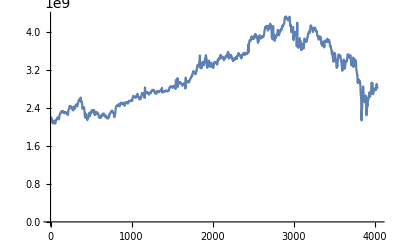

```mathematica
ListLinePlot[twapsWethUsdc90dFiltered4Week, PlotRange->All]
```

```mathematica
twapsWethUsdc90dFiltered6Week = Table[twapsWethUsdc90dFiltered[[i]], {i, 1, 6*6*24*7}]
```

{2.20799×10^9,2.20533×10^9,2.20572×10^9,2.20558×10^9,2.20476×10^9,2.2039×10^9,2.20513×10^9,2.2031×10^9,2.1997×10^9,2.1977×10^9,2.19642×10^9,2.19264×10^9,2.18452×10^9,2.17974×10^9,2.17409×10^9,2.16595×10^9,2.15763×10^9,2.14687×10^9,2.13229×10^9,2.11795×10^9,2.10658×10^9,2.10155×10^9,2.10459×10^9,2.10836×10^9,2.11006×10^9,2.10998×10^9,2.10671×10^9,2.09959×10^9,2.09156×10^9,2.08485×10^9,2.07922×10^9,2.07646×10^9,2.07685×10^9,2.08201×10^9,2.08605×10^9,2.0936×10^9,2.09635×10^9,2.10078×10^9,2.1063×10^9,2.11173×10^9,2.11541×10^9,2.12081×10^9,2.12707×10^9,2.13185×10^9,2.13614×10^9,2.13829×10^9,2.1356×10^9,2.13202×10^9,2.12948×10^9,2.12444×10^9,2.12109×10^9,2.11405×10^9,2.10656×10^9,2.09709×10^9,2.08876×10^9,2.08203×10^9,2.07571×10^9,2.076×10^9,2.07804×10^9,2.0826×10^9,2.092×10^9,2.10137×10^9,2.11342×10^9,2.12133×10^9,2.133×10^9,2.13803×10^9,2.14019×10^9,2.14584×10^9,2.14715×10^9,2.14686×10^9,2.14686×10^9,2.14853×10^9,2.15282×10^9,2.15936×10^9,2.16644×10^9,2.17366×10^9,2.18035×10^9,2.18508×10^9,2.18679×10^9,2.18661×10^9,2.18817×10^9,2.18892×10^9,2.18838×10^9,2.18555×10^9,2.18398×10^9,2.18084×10^9,2.17902×10^9,2.1791×10^9,2.18103×10^9,2.18514×10^9,2.19238×10^9,2.1997×10^9,2.20797×10^9,2.21494×10^9,2.21708×10^9,2.21531×10^9,2.20923×10^9,2.20054×10^9,2.19002×10^9,2.1798×10^9,2.17015×10^9,2.16504×10^9,2.16313×10^9,2.16575×10^9,2.17722×10^9,2.18669×10^9,2.20064×10^9,2.21318×10^9,2.2252×10^9,2.23608×10^9,2.24299×10^9,2.25221×10^9,2.25492×10^9,2.25937×10^9,2.2656×10^9,2.26918×10^9,2.27751×10^9,2.28222×10^9,2.28527×10^9,2.28614×10^9,2.28598×10^9,2.28635×10^9,2.29055×10^9,2.29529×10^9,2.30221×10^9,2.30863×10^9,2.31448×10^9,2.31796×10^9,2.31814×10^9,2.31637×10^9,2.31586×10^9,2.3173×10^9,2.31787×10^9,2.32308×10^9,2.32914×10^9,2.33406×10^9,2.33557×10^9,2.3385×10^9,2.33849×10^9,2.33491×10^9,2.33032×10^9,2.32851×10^9,2.32627×10^9,2.32693×10^9,2.327×10^9,2.32861×10^9,2.32872×10^9,2.3323×10^9,2.33609×10^9,2.34017×10^9,2.34079×10^9,2.33792×10^9,2.32664×10^9,2.31713×10^9,2.30791×10^9,2.30481×10^9,2.30593×10^9,2.31122×10^9,2.31633×10^9,2.31671×10^9,2.31654×10^9,2.31869×10^9,2.31917×10^9,2.32151×10^9,2.32353×10^9,2.32558×10^9,2.32512×10^9,2.32216×10^9,2.31566×10^9,2.30797×10^9,2.30158×10^9,2.30019×10^9,2.29582×10^9,2.29745×10^9,2.29969×10^9,2.3025×10^9,2.30329×10^9,2.30422×10^9,2.30287×10^9,2.3013×10^9,2.30039×10^9,2.30185×10^9,2.30393×10^9,2.30631×10^9,2.31256×10^9,2.31628×10^9,2.31432×10^9,2.31156×10^9,2.30752×10^9,2.30176×10^9,2.29729×10^9,2.29414×10^9,2.2911×10^9,2.28937×10^9,2.28748×10^9,2.28608×10^9,2.2887×10^9,2.29112×10^9,2.29267×10^9,2.29639×10^9,2.29873×10^9,2.30062×10^9,2.30202×10^9,2.3014×10^9,2.29931×10^9,2.29393×10^9,2.28801×10^9,2.28086×10^9,2.27559×10^9,2.27101×10^9,2.26585×10^9,2.26218×10^9,2.25884×10^9,2.25879×10^9,2.26032×10^9,2.27399×10^9,2.28924×10^9,2.31057×10^9,2.32906×10^9,2.35018×10^9,2.35935×10^9,2.36454×10^9,2.36951×10^9,2.37057×10^9,2.37302×10^9,2.37608×10^9,2.37666×10^9,2.37942×10^9,2.38804×10^9,2.3999×10^9,2.41264×10^9,2.42281×10^9,2.43272×10^9,2.43379×10^9,2.43288×10^9,2.43142×10^9,2.43641×10^9,2.44261×10^9,2.44738×10^9,2.44744×10^9,2.44522×10^9,2.43939×10^9,2.43497×10^9,2.43264×10^9,2.42861×10^9,2.42458×10^9,2.42349×10^9,2.42339×10^9,2.42106×10^9,2.41978×10^9,2.41792×10^9,2.41518×10^9,2.41306×10^9,2.41496×10^9,2.42005×10^9,2.42622×10^9,2.43092×10^9,2.43237×10^9,2.43004×10^9,2.42582×10^9,2.42046×10^9,2.41259×10^9,2.40775×10^9,2.40375×10^9,2.39108×10^9,2.39655×10^9,2.3956×10^9,2.39224×10^9,2.38944×10^9,2.39842×10^9,2.38836×10^9,2.38184×10^9,2.3781×10^9,2.3728×10^9,2.36321×10^9,2.35704×10^9,2.35824×10^9,2.36068×10^9,2.3603×10^9,2.36015×10^9,2.3579×10^9,2.35752×10^9,2.35909×10^9,2.36502×10^9,2.37908×10^9,2.39834×10^9,2.4127×10^9,2.42598×10^9,2.43401×10^9,2.43222×10^9,2.41886×10^9,2.40246×10^9,2.39316×10^9,2.38761×10^9,2.38868×10^9,2.40099×10^9,2.41134×10^9,2.41463×10^9,2.41221×10^9,2.40891×10^9,2.40558×10^9,2.40312×10^9,2.40413×10^9,2.41017×10^9,2.41718×10^9,2.4245×10^9,2.43149×10^9,2.43396×10^9,2.43713×10^9,2.43943×10^9,2.44341×10^9,2.45213×10^9,2.45836×10^9,2.47155×10^9,2.47967×10^9,2.48092×10^9,2.48045×10^9,2.47832×10^9,2.47252×10^9,2.46923×10^9,2.46871×10^9,2.46728×10^9,2.46567×10^9,2.46427×10^9,2.45963×10^9,2.45423×10^9,2.44689×10^9,2.44154×10^9,2.43926×10^9,2.44175×10^9,2.44538×10^9,2.45511×10^9,2.46241×10^9,2.47271×10^9,2.47959×10^9,2.48489×10^9,2.48836×10^9,2.49389×10^9,2.49936×10^9,2.50627×10^9,2.51533×10^9,2.52654×10^9,2.53708×10^9,2.54547×10^9,2.55359×10^9,2.56074×10^9,2.5665×10^9,2.57023×10^9,2.57431×10^9,2.57599×10^9,2.57284×10^9,2.57025×10^9,2.56978×10^9,2.56996×10^9,2.56804×10^9,2.56612×10^9,2.56696×10^9,2.56592×10^9,2.56733×10^9,2.57437×10^9,2.58211×10^9,2.58779×10^9,2.59054×10^9,2.59214×10^9,2.59185×10^9,2.59371×10^9,2.59943×10^9,2.60624×10^9,2.61565×10^9,2.6257×10^9,2.62317×10^9,2.61751×10^9,2.60893×10^9,2.59826×10^9,2.56573×10^9,2.55281×10^9,2.54389×10^9,2.54209×10^9,2.54473×10^9,2.54821×10^9,2.54514×10^9,2.53653×10^9,2.52562×10^9,2.51813×10^9,2.5154×10^9,2.51558×10^9,2.51916×10^9,2.51323×10^9,2.49936×10^9,2.48124×10^9,2.45851×10^9,2.42959×10^9,2.40366×10^9,2.39405×10^9,2.38788×10^9,2.38704×10^9,2.39695×10^9,2.41192×10^9,2.41702×10^9,2.41739×10^9,2.4192×10^9,2.41777×10^9,2.4136×10^9,2.41326×10^9,2.4183×10^9,2.42198×10^9,2.42571×10^9,2.42369×10^9,2.41881×10^9,2.41632×10^9,2.417×10^9,2.41421×10^9,2.41041×10^9,2.40525×10^9,2.39325×10^9,2.3742×10^9,2.35997×10^9,2.34364×10^9,2.33289×10^9,2.31322×10^9,2.28152×10^9,2.25267×10^9,2.2342×10^9,2.21876×10^9,2.21877×10^9,2.20542×10^9,2.24012×10^9,2.25011×10^9,2.25639×10^9,2.26274×10^9,2.28594×10^9,2.25998×10^9,2.25792×10^9,2.24987×10^9,2.23585×10^9,2.23095×10^9,2.21622×10^9,2.20627×10^9,2.20518×10^9,2.20774×10^9,2.20858×10^9,2.21536×10^9,2.21222×10^9,2.201×10^9,2.19372×10^9,2.18937×10^9,2.1898×10^9,2.19679×10^9,2.19911×10^9,2.1922×10^9,2.1814×10^9,2.16775×10^9,2.15329×10^9,2.14905×10^9,2.15453×10^9,2.16311×10^9,2.17754×10^9,2.1886×10^9,2.19496×10^9,2.19521×10^9,2.19642×10^9,2.19586×10^9,2.20198×10^9,2.21422×10^9,2.22915×10^9,2.24864×10^9,2.26186×10^9,2.26818×10^9,2.27401×10^9,2.27947×10^9,2.28488×10^9,2.28763×10^9,2.29374×10^9,2.2935×10^9,2.28949×10^9,2.28122×10^9,2.27718×10^9,2.26861×10^9,2.26267×10^9,2.25558×10^9,2.24668×10^9,2.23444×10^9,2.22963×10^9,2.22708×10^9,2.23103×10^9,2.2414×10^9,2.25694×10^9,2.26796×10^9,2.27638×10^9,2.28157×10^9,2.28064×10^9,2.28194×10^9,2.28855×10^9,2.29747×10^9,2.30827×10^9,2.32178×10^9,2.32668×10^9,2.33208×10^9,2.33238×10^9,2.3302×10^9,2.32706×10^9,2.32483×10^9,2.31294×10^9,2.30725×10^9,2.30586×10^9,2.30549×10^9,2.30875×10^9,2.32069×10^9,2.3289×10^9,2.33887×10^9,2.34455×10^9,2.34705×10^9,2.34831×10^9,2.34906×10^9,2.35316×10^9,2.35714×10^9,2.35986×10^9,2.36222×10^9,2.3601×10^9,2.3539×10^9,2.34852×10^9,2.34723×10^9,2.34445×10^9,2.34153×10^9,2.33929×10^9,2.33339×10^9,2.32678×10^9,2.32081×10^9,2.31699×10^9,2.31726×10^9,2.32052×10^9,2.32377×10^9,2.32889×10^9,2.33394×10^9,2.33811×10^9,2.34591×10^9,2.35097×10^9,2.3484×10^9,2.35168×10^9,2.32961×10^9,2.31129×10^9,2.29316×10^9,2.28242×10^9,2.26549×10^9,2.27423×10^9,2.27616×10^9,2.27699×10^9,2.27214×10^9,2.26531×10^9,2.26117×10^9,2.26262×10^9,2.26374×10^9,2.27259×10^9,2.28756×10^9,2.29605×10^9,2.30558×10^9,2.31085×10^9,2.31211×10^9,2.30824×10^9,2.30791×10^9,2.30698×10^9,2.30738×10^9,2.30927×10^9,2.31281×10^9,2.31167×10^9,2.31119×10^9,2.31043×10^9,2.31036×10^9,2.31235×10^9,2.31484×10^9,2.31729×10^9,2.31702×10^9,2.31256×10^9,2.30616×10^9,2.30047×10^9,2.29057×10^9,2.28115×10^9,2.27844×10^9,2.27622×10^9,2.27517×10^9,2.27651×10^9,2.28024×10^9,2.2841×10^9,2.28743×10^9,2.29157×10^9,2.29036×10^9,2.28662×10^9,2.2796×10^9,2.27321×10^9,2.26679×10^9,2.26409×10^9,2.25823×10^9,2.25215×10^9,2.24222×10^9,2.2328×10^9,2.22194×10^9,2.21341×10^9,2.20809×10^9,2.20552×10^9,2.20414×10^9,2.19895×10^9,2.19647×10^9,2.19691×10^9,2.19647×10^9,2.19503×10^9,2.20427×10^9,2.21535×10^9,2.2193×10^9,2.22389×10^9,2.22751×10^9,2.22651×10^9,2.22377×10^9,2.22182×10^9,2.21675×10^9,2.21353×10^9,2.2085×10^9,2.2066×10^9,2.2045×10^9,2.20086×10^9,2.20024×10^9,2.20296×10^9,2.2091×10^9,2.21676×10^9,2.23307×10^9,2.24249×10^9,2.24753×10^9,2.25021×10^9,2.24966×10^9,2.24755×10^9,2.2456×10^9,2.23852×10^9,2.23414×10^9,2.2323×10^9,2.23331×10^9,2.23724×10^9,2.25193×10^9,2.26192×10^9,2.2681×10^9,2.27309×10^9,2.27821×10^9,2.27709×10^9,2.27605×10^9,2.2762×10^9,2.27657×10^9,2.2759×10^9,2.27331×10^9,2.27229×10^9,2.27357×10^9,2.27615×10^9,2.27991×10^9,2.28524×10^9,2.28907×10^9,2.28996×10^9,2.28935×10^9,2.28902×10^9,2.28737×10^9,2.28427×10^9,2.28126×10^9,2.27787×10^9,2.2695×10^9,2.2637×10^9,2.25955×10^9,2.25705×10^9,2.25289×10^9,2.24485×10^9,2.23883×10^9,2.23579×10^9,2.23314×10^9,2.22735×10^9,2.22636×10^9,2.22483×10^9,2.22245×10^9,2.2202×10^9,2.22366×10^9,2.22793×10^9,2.23311×10^9,2.23822×10^9,2.24126×10^9,2.2419×10^9,2.2428×10^9,2.2431×10^9,2.24391×10^9,2.24438×10^9,2.24251×10^9,2.23764×10^9,2.23285×10^9,2.22346×10^9,2.21278×10^9,2.20363×10^9,2.19764×10^9,2.19271×10^9,2.18978×10^9,2.18801×10^9,2.18846×10^9,2.18976×10^9,2.19189×10^9,2.19508×10^9,2.19872×10^9,2.19979×10^9,2.20061×10^9,2.20091×10^9,2.20067×10^9,2.20039×10^9,2.19911×10^9,2.19718×10^9,2.19265×10^9,2.18857×10^9,2.18462×10^9,2.18244×10^9,2.18365×10^9,2.18494×10^9,2.18744×10^9,2.19216×10^9,2.19477×10^9,2.20087×10^9,2.20936×10^9,2.21653×10^9,2.22071×10^9,2.2223×10^9,2.2192×10^9,2.22228×10^9,2.22865×10^9,2.23954×10^9,2.25415×10^9,2.26709×10^9,2.27141×10^9,2.27257×10^9,2.26885×10^9,2.26645×10^9,2.26725×10^9,2.26852×10^9,2.27247×10^9,2.27791×10^9,2.28419×10^9,2.29287×10^9,2.29906×10^9,2.30388×10^9,2.30929×10^9,2.31112×10^9,2.31317×10^9,2.31564×10^9,2.31573×10^9,2.31561×10^9,2.31542×10^9,2.31413×10^9,2.31519×10^9,2.31908×10^9,2.32147×10^9,2.32736×10^9,2.33494×10^9,2.33998×10^9,2.34386×10^9,2.34424×10^9,2.34487×10^9,2.34497×10^9,2.34218×10^9,2.34076×10^9,2.3418×10^9,2.34242×10^9,2.34246×10^9,2.34516×10^9,2.34479×10^9,2.34044×10^9,2.33679×10^9,2.33343×10^9,2.3292×10^9,2.32519×10^9,2.32298×10^9,2.31663×10^9,2.30992×10^9,2.3041×10^9,2.29961×10^9,2.29866×10^9,2.29799×10^9,2.29939×10^9,2.2985×10^9,2.29236×10^9,2.28655×10^9,2.28392×10^9,2.2809×10^9,2.27635×10^9,2.26595×10^9,2.25331×10^9,2.24366×10^9,2.22887×10^9,2.2145×10^9,2.21107×10^9,2.21254×10^9,2.21443×10^9,2.22275×10^9,2.23622×10^9,2.24861×10^9,2.2594×10^9,2.26408×10^9,2.27033×10^9,2.2803×10^9,2.28652×10^9,2.29094×10^9,2.2981×10^9,2.31555×10^9,2.3368×10^9,2.35786×10^9,2.3769×10^9,2.39538×10^9,2.40696×10^9,2.41176×10^9,2.41569×10^9,2.42174×10^9,2.42885×10^9,2.4366×10^9,2.44476×10^9,2.44712×10^9,2.44617×10^9,2.44403×10^9,2.44363×10^9,2.44219×10^9,2.44623×10^9,2.44958×10^9,2.45123×10^9,2.45112×10^9,2.45167×10^9,2.45407×10^9,2.45812×10^9,2.46162×10^9,2.46369×10^9,2.46427×10^9,2.46289×10^9,2.45751×10^9,2.45375×10^9,2.45255×10^9,2.4526×10^9,2.45302×10^9,2.45883×10^9,2.46523×10^9,2.47045×10^9,2.47648×10^9,2.48128×10^9,2.48101×10^9,2.47698×10^9,2.47104×10^9,2.46507×10^9,2.46046×10^9,2.45761×10^9,2.45548×10^9,2.45276×10^9,2.44984×10^9,2.44595×10^9,2.44291×10^9,2.44226×10^9,2.44154×10^9,2.43928×10^9,2.43783×10^9,2.44323×10^9,2.45125×10^9,2.45873×10^9,2.47179×10^9,2.48318×10^9,2.48587×10^9,2.48714×10^9,2.48866×10^9,2.49182×10^9,2.49573×10^9,2.50131×10^9,2.50888×10^9,2.51503×10^9,2.51715×10^9,2.51551×10^9,2.5143×10^9,2.51203×10^9,2.50693×10^9,2.50391×10^9,2.49954×10^9,2.49506×10^9,2.49414×10^9,2.49543×10^9,2.49693×10^9,2.4989×10^9,2.49877×10^9,2.49364×10^9,2.49147×10^9,2.48988×10^9,2.48811×10^9,2.48799×10^9,2.48933×10^9,2.49132×10^9,2.49484×10^9,2.49545×10^9,2.49487×10^9,2.48933×10^9,2.48526×10^9,2.48001×10^9,2.48286×10^9,2.49015×10^9,2.50192×10^9,2.50791×10^9,2.51492×10^9,2.51568×10^9,2.51417×10^9,2.50893×10^9,2.50468×10^9,2.50156×10^9,2.49831×10^9,2.49638×10^9,2.49477×10^9,2.49335×10^9,2.49183×10^9,2.49079×10^9,2.48908×10^9,2.48649×10^9,2.48389×10^9,2.48105×10^9,2.47142×10^9,2.46433×10^9,2.45583×10^9,2.45223×10^9,2.45422×10^9,2.46197×10^9,2.47306×10^9,2.4924×10^9,2.50467×10^9,2.51184×10^9,2.51584×10^9,2.51972×10^9,2.51729×10^9,2.51696×10^9,2.51681×10^9,2.51826×10^9,2.52155×10^9,2.52454×10^9,2.52341×10^9,2.52264×10^9,2.52008×10^9,2.51702×10^9,2.51238×10^9,2.51208×10^9,2.51191×10^9,2.51242×10^9,2.51245×10^9,2.5126×10^9,2.51481×10^9,2.51713×10^9,2.51884×10^9,2.52143×10^9,2.5239×10^9,2.52503×10^9,2.52365×10^9,2.51914×10^9,2.51419×10^9,2.50823×10^9,2.50277×10^9,2.49839×10^9,2.49751×10^9,2.49796×10^9,2.49829×10^9,2.49901×10^9,2.50106×10^9,2.50468×10^9,2.50984×10^9,2.51568×10^9,2.52184×10^9,2.52488×10^9,2.52826×10^9,2.53554×10^9,2.53955×10^9,2.54475×10^9,2.54931×10^9,2.55421×10^9,2.55606×10^9,2.55704×10^9,2.558×10^9,2.55742×10^9,2.55613×10^9,2.55383×10^9,2.55188×10^9,2.55033×10^9,2.55004×10^9,2.54953×10^9,2.54977×10^9,2.54832×10^9,2.54754×10^9,2.547×10^9,2.54779×10^9,2.54815×10^9,2.5505×10^9,2.55165×10^9,2.55143×10^9,2.55092×10^9,2.55027×10^9,2.54893×10^9,2.54858×10^9,2.55059×10^9,2.553×10^9,2.55592×10^9,2.55994×10^9,2.56424×10^9,2.56771×10^9,2.57182×10^9,2.57375×10^9,2.57396×10^9,2.57164×10^9,2.56896×10^9,2.56596×10^9,2.5636×10^9,2.56107×10^9,2.55891×10^9,2.5563×10^9,2.55368×10^9,2.55618×10^9,2.56814×10^9,2.57934×10^9,2.59744×10^9,2.61451×10^9,2.62719×10^9,2.63082×10^9,2.6356×10^9,2.64104×10^9,2.64795×10^9,2.65163×10^9,2.65855×10^9,2.65906×10^9,2.65748×10^9,2.65239×10^9,2.65007×10^9,2.64537×10^9,2.6422×10^9,2.63909×10^9,2.63922×10^9,2.63904×10^9,2.63858×10^9,2.63735×10^9,2.63764×10^9,2.63803×10^9,2.63722×10^9,2.63794×10^9,2.6394×10^9,2.63626×10^9,2.6309×10^9,2.62599×10^9,2.62427×10^9,2.62282×10^9,2.62459×10^9,2.62923×10^9,2.63363×10^9,2.63453×10^9,2.63619×10^9,2.63742×10^9,2.6365×10^9,2.63813×10^9,2.63956×10^9,2.63923×10^9,2.63813×10^9,2.63675×10^9,2.63277×10^9,2.62774×10^9,2.6252×10^9,2.62523×10^9,2.62802×10^9,2.63213×10^9,2.63998×10^9,2.65069×10^9,2.66276×10^9,2.67138×10^9,2.67884×10^9,2.6839×10^9,2.68591×10^9,2.68649×10^9,2.68838×10^9,2.69162×10^9,2.69579×10^9,2.69895×10^9,2.70219×10^9,2.70203×10^9,2.6985×10^9,2.69107×10^9,2.68116×10^9,2.6707×10^9,2.65959×10^9,2.65079×10^9,2.6437×10^9,2.64043×10^9,2.63928×10^9,2.63988×10^9,2.6411×10^9,2.64281×10^9,2.6419×10^9,2.63996×10^9,2.63913×10^9,2.63692×10^9,2.63059×10^9,2.629×10^9,2.62375×10^9,2.6125×10^9,2.6043×10^9,2.59472×10^9,2.59248×10^9,2.58477×10^9,2.58679×10^9,2.59057×10^9,2.5975×10^9,2.60157×10^9,2.60817×10^9,2.61214×10^9,2.61509×10^9,2.61697×10^9,2.61809×10^9,2.61915×10^9,2.61857×10^9,2.61463×10^9,2.60977×10^9,2.60421×10^9,2.6001×10^9,2.60019×10^9,2.60194×10^9,2.60676×10^9,2.61245×10^9,2.61714×10^9,2.62146×10^9,2.62891×10^9,2.63716×10^9,2.64614×10^9,2.65821×10^9,2.67367×10^9,2.68377×10^9,2.69346×10^9,2.70188×10^9,2.70791×10^9,2.71172×10^9,2.71441×10^9,2.71902×10^9,2.71242×10^9,2.70675×10^9,2.70174×10^9,2.69608×10^9,2.69353×10^9,2.69857×10^9,2.7032×10^9,2.70851×10^9,2.71255×10^9,2.71347×10^9,2.71033×10^9,2.70519×10^9,2.69555×10^9,2.68986×10^9,2.68374×10^9,2.68337×10^9,2.68503×10^9,2.68906×10^9,2.69365×10^9,2.70085×10^9,2.7055×10^9,2.71066×10^9,2.71477×10^9,2.71774×10^9,2.71978×10^9,2.71976×10^9,2.71957×10^9,2.72293×10^9,2.72605×10^9,2.72826×10^9,2.61748×10^9,2.72971×10^9,2.72785×10^9,2.72473×10^9,2.72449×10^9,2.83875×10^9,2.73048×10^9,2.70685×10^9,2.72574×10^9,2.72363×10^9,2.71831×10^9,2.71326×10^9,2.73625×10^9,2.71169×10^9,2.71164×10^9,2.71516×10^9,2.72376×10^9,2.73414×10^9,2.74182×10^9,2.74377×10^9,2.74286×10^9,2.73679×10^9,2.72737×10^9,2.72313×10^9,2.72223×10^9,2.72211×10^9,2.72412×10^9,2.73119×10^9,2.73578×10^9,2.73961×10^9,2.74275×10^9,2.74377×10^9,2.74148×10^9,2.73802×10^9,2.73215×10^9,2.72686×10^9,2.72274×10^9,2.71851×10^9,2.71589×10^9,2.71682×10^9,2.71852×10^9,2.71973×10^9,2.72099×10^9,2.72118×10^9,2.72036×10^9,2.71803×10^9,2.71711×10^9,2.71625×10^9,2.71402×10^9,2.7077×10^9,2.70253×10^9,2.69641×10^9,2.69104×10^9,2.68881×10^9,2.6873×10^9,2.68706×10^9,2.68928×10^9,2.69198×10^9,2.69406×10^9,2.69883×10^9,2.70389×10^9,2.70778×10^9,2.71183×10^9,2.71527×10^9,2.72096×10^9,2.72397×10^9,2.72755×10^9,2.72925×10^9,2.72992×10^9,2.73064×10^9,2.73154×10^9,2.73126×10^9,2.73096×10^9,2.7294×10^9,2.72633×10^9,2.724×10^9,2.72102×10^9,2.71824×10^9,2.72097×10^9,2.72841×10^9,2.73666×10^9,2.74697×10^9,2.75731×10^9,2.7641×10^9,2.76504×10^9,2.76546×10^9,2.76513×10^9,2.76459×10^9,2.76491×10^9,2.76668×10^9,2.76743×10^9,2.76769×10^9,2.76806×10^9,2.76717×10^9,2.76543×10^9,2.76721×10^9,2.77086×10^9,2.775×10^9,2.78064×10^9,2.78663×10^9,2.78752×10^9,2.78625×10^9,2.78341×10^9,2.77901×10^9,2.77219×10^9,2.76783×10^9,2.76488×10^9,2.76346×10^9,2.7638×10^9,2.76513×10^9,2.7666×10^9,2.76932×10^9,2.77417×10^9,2.77752×10^9,2.78108×10^9,2.7845×10^9,2.78344×10^9,2.77817×10^9,2.77243×10^9,2.76555×10^9,2.75762×10^9,2.74739×10^9,2.74127×10^9,2.738×10^9,2.7346×10^9,2.73519×10^9,2.73259×10^9,2.72757×10^9,2.72235×10^9,2.7184×10^9,2.71327×10^9,2.71615×10^9,2.71967×10^9,2.72248×10^9,2.72501×10^9,2.72742×10^9,2.72738×10^9,2.72296×10^9,2.71582×10^9,2.71306×10^9,2.71057×10^9,2.70641×10^9,2.70649×10^9,2.70927×10^9,2.7094×10^9,2.70879×10^9,2.71196×10^9,2.71795×10^9,2.72507×10^9,2.73315×10^9,2.74055×10^9,2.74832×10^9,2.7532×10^9,2.75747×10^9,2.76008×10^9,2.76143×10^9,2.76196×10^9,2.76191×10^9,2.76149×10^9,2.75977×10^9,2.7548×10^9,2.75368×10^9,2.75089×10^9,2.7477×10^9,2.74435×10^9,2.74318×10^9,2.73905×10^9,2.73823×10^9,2.73931×10^9,2.74195×10^9,2.74371×10^9,2.74567×10^9,2.74399×10^9,2.74219×10^9,2.7421×10^9,2.74112×10^9,2.74029×10^9,2.74087×10^9,2.74219×10^9,2.74109×10^9,2.7422×10^9,2.74414×10^9,2.74721×10^9,2.75003×10^9,2.75336×10^9,2.75674×10^9,2.75873×10^9,2.76045×10^9,2.76198×10^9,2.7632×10^9,2.76403×10^9,2.76461×10^9,2.76565×10^9,2.76728×10^9,2.77046×10^9,2.77379×10^9,2.77742×10^9,2.78123×10^9,2.78293×10^9,2.7827×10^9,2.78245×10^9,2.78097×10^9,2.77977×10^9,2.77746×10^9,2.77616×10^9,2.77466×10^9,2.77401×10^9,2.77533×10^9,2.7787×10^9,2.78216×10^9,2.80134×10^9,2.78906×10^9,2.78842×10^9,2.78723×10^9,2.82806×10^9,2.76798×10^9,2.78159×10^9,2.7813×10^9,2.77825×10^9,2.72922×10^9,2.76753×10^9,2.76317×10^9,2.75753×10^9,2.75353×10^9,2.75102×10^9,2.7483×10^9,2.74567×10^9,2.74392×10^9,2.74468×10^9,2.74638×10^9,2.74819×10^9,2.7477×10^9,2.74719×10^9,2.74595×10^9,2.74403×10^9,2.74128×10^9,2.74355×10^9,2.74612×10^9,2.7494×10^9,2.75331×10^9,2.75533×10^9,2.75248×10^9,2.7507×10^9,2.74822×10^9,2.74593×10^9,2.7459×10^9,2.74559×10^9,2.74579×10^9,2.74671×10^9,2.74729×10^9,2.7484×10^9,2.75239×10^9,2.75614×10^9,2.75919×10^9,2.76152×10^9,2.7637×10^9,2.76366×10^9,2.76471×10^9,2.76466×10^9,2.76468×10^9,2.76518×10^9,2.76498×10^9,2.76413×10^9,2.76529×10^9,2.76855×10^9,2.77194×10^9,2.77473×10^9,2.77689×10^9,2.77822×10^9,2.77799×10^9,2.77618×10^9,2.77409×10^9,2.77224×10^9,2.76982×10^9,2.76719×10^9,2.7649×10^9,2.7613×10^9,2.75929×10^9,2.75776×10^9,2.75645×10^9,2.75597×10^9,2.75652×10^9,2.75541×10^9,2.7544×10^9,2.75292×10^9,2.75267×10^9,2.75227×10^9,2.7536×10^9,2.75607×10^9,2.75943×10^9,2.76309×10^9,2.76715×10^9,2.76933×10^9,2.77048×10^9,2.77078×10^9,2.77071×10^9,2.76979×10^9,2.76909×10^9,2.76776×10^9,2.76768×10^9,2.76883×10^9,2.77949×10^9,2.79242×10^9,2.80527×10^9,2.81563×10^9,2.82967×10^9,2.83186×10^9,2.83186×10^9,2.83116×10^9,2.83322×10^9,2.83502×10^9,2.83731×10^9,2.8405×10^9,2.84328×10^9,2.84375×10^9,2.84361×10^9,2.84323×10^9,2.84274×10^9,2.84259×10^9,2.84563×10^9,2.85031×10^9,2.85527×10^9,2.85864×10^9,2.86233×10^9,2.86076×10^9,2.85856×10^9,2.85557×10^9,2.85439×10^9,2.85513×10^9,2.85625×10^9,2.85655×10^9,2.85682×10^9,2.85649×10^9,2.85557×10^9,2.85521×10^9,2.85615×10^9,2.85757×10^9,2.85818×10^9,2.8577×10^9,2.85372×10^9,2.84594×10^9,2.83934×10^9,2.83444×10^9,2.8325×10^9,2.83316×10^9,2.83598×10^9,2.8374×10^9,2.83687×10^9,2.83468×10^9,2.83461×10^9,2.83743×10^9,2.84098×10^9,2.84543×10^9,2.84947×10^9,2.8527×10^9,2.854×10^9,2.8552×10^9,2.85894×10^9,2.8634×10^9,2.86716×10^9,2.87105×10^9,2.87345×10^9,2.87385×10^9,2.87273×10^9,2.87143×10^9,2.86996×10^9,2.86907×10^9,2.86878×10^9,2.86857×10^9,2.86782×10^9,2.86742×10^9,2.86603×10^9,2.8637×10^9,2.86046×10^9,2.85818×10^9,2.85434×10^9,2.8527×10^9,2.85328×10^9,2.85804×10^9,2.86276×10^9,2.86969×10^9,2.87547×10^9,2.80645×10^9,2.88817×10^9,2.89516×10^9,2.90277×10^9,2.90995×10^9,2.99492×10^9,2.92215×10^9,2.92512×10^9,2.9281×10^9,2.93023×10^9,2.93112×10^9,2.9317×10^9,2.93274×10^9,2.93337×10^9,2.93337×10^9,2.93266×10^9,2.92963×10^9,2.92575×10^9,2.92503×10^9,2.92361×10^9,2.9247×10^9,2.9292×10^9,2.93421×10^9,2.93769×10^9,3.03478×10^9,2.93804×10^9,2.93441×10^9,2.93127×10^9,2.92849×10^9,2.84973×10^9,2.9289×10^9,2.93166×10^9,2.93378×10^9,2.93654×10^9,2.93757×10^9,2.93919×10^9,2.94188×10^9,2.94373×10^9,2.94649×10^9,2.94615×10^9,2.94533×10^9,2.94334×10^9,2.9416×10^9,2.93936×10^9,2.93819×10^9,2.93651×10^9,2.93576×10^9,2.93568×10^9,2.93596×10^9,2.93709×10^9,2.93933×10^9,2.94297×10^9,2.94542×10^9,2.94764×10^9,2.94994×10^9,2.95137×10^9,2.9515×10^9,2.95024×10^9,2.94409×10^9,2.93685×10^9,2.92533×10^9,2.91281×10^9,2.91113×10^9,2.91184×10^9,2.91191×10^9,2.91431×10^9,2.91738×10^9,2.91731×10^9,2.91522×10^9,2.91575×10^9,2.91633×10^9,2.9172×10^9,2.91769×10^9,2.91803×10^9,2.91747×10^9,2.91558×10^9,2.90994×10^9,2.90433×10^9,2.89991×10^9,2.89507×10^9,2.89195×10^9,2.88844×10^9,2.88498×10^9,2.87998×10^9,2.87532×10^9,2.87316×10^9,2.87376×10^9,2.875×10^9,2.87711×10^9,2.87898×10^9,2.88206×10^9,2.88564×10^9,2.89221×10^9,2.89905×10^9,2.90687×10^9,2.91168×10^9,2.9154×10^9,2.91581×10^9,2.91519×10^9,2.91474×10^9,2.91469×10^9,2.91541×10^9,2.91761×10^9,2.9211×10^9,2.92439×10^9,2.92719×10^9,2.92829×10^9,2.92738×10^9,2.92673×10^9,2.92583×10^9,2.92599×10^9,2.92453×10^9,2.92212×10^9,2.92077×10^9,2.91849×10^9,2.9166×10^9,2.9168×10^9,2.91798×10^9,2.91889×10^9,2.91928×10^9,2.91902×10^9,2.81586×10^9,2.91997×10^9,2.92207×10^9,2.92466×10^9,2.92757×10^9,3.04472×10^9,2.93313×10^9,2.93374×10^9,2.93474×10^9,2.93518×10^9,2.93494×10^9,2.93477×10^9,2.93473×10^9,2.93493×10^9,2.93632×10^9,2.938×10^9,2.94001×10^9,2.94144×10^9,2.94487×10^9,2.94892×10^9,2.95266×10^9,2.9592×10^9,2.96545×10^9,2.96951×10^9,2.97281×10^9,2.97447×10^9,2.97448×10^9,2.97352×10^9,2.97196×10^9,2.97037×10^9,2.96885×10^9,2.96757×10^9,2.96789×10^9,2.96959×10^9,2.97161×10^9,2.97374×10^9,2.97396×10^9,2.97038×10^9,2.96509×10^9,2.95729×10^9,2.94817×10^9,2.94357×10^9,2.94192×10^9,2.94294×10^9,2.94426×10^9,2.94644×10^9,2.95175×10^9,2.95794×10^9,2.96718×10^9,2.97438×10^9,2.98319×10^9,2.98637×10^9,2.98854×10^9,2.99013×10^9,2.99205×10^9,2.99826×10^9,3.00421×10^9,3.00858×10^9,3.01404×10^9,3.01764×10^9,3.01749×10^9,3.01875×10^9,3.02059×10^9,3.02486×10^9,3.02954×10^9,3.03463×10^9,3.03939×10^9,3.04473×10^9,3.04978×10^9,3.05285×10^9,3.0543×10^9,3.05471×10^9,3.0537×10^9,3.05238×10^9,3.05422×10^9,3.05571×10^9,3.06099×10^9,3.0702×10^9,3.08027×10^9,3.08642×10^9,3.08984×10^9,3.09292×10^9,3.09329×10^9,3.09247×10^9,3.09069×10^9,3.0893×10^9,3.09236×10^9,3.10229×10^9,3.11249×10^9,3.12166×10^9,3.13349×10^9,3.14192×10^9,3.14816×10^9,3.1563×10^9,3.16645×10^9,3.17416×10^9,3.17874×10^9,3.1755×10^9,3.17232×10^9,3.16874×10^9,3.16586×10^9,3.16861×10^9,3.16742×10^9,3.16414×10^9,3.1593×10^9,3.15435×10^9,3.14781×10^9,3.14722×10^9,3.14946×10^9,3.15466×10^9,3.15986×10^9,3.16539×10^9,3.16726×10^9,3.16749×10^9,3.16459×10^9,3.15916×10^9,3.1508×10^9,3.14581×10^9,3.14291×10^9,3.13797×10^9,3.13545×10^9,3.13475×10^9,3.12745×10^9,3.12068×10^9,3.11636×10^9,3.11706×10^9,3.11962×10^9,3.12807×10^9,3.14131×10^9,3.1519×10^9,3.15746×10^9,3.1652×10^9,3.17054×10^9,3.17034×10^9,3.17038×10^9,3.17194×10^9,3.17099×10^9,3.16982×10^9,3.17997×10^9,3.19805×10^9,3.21332×10^9,3.2328×10^9,3.25006×10^9,3.26408×10^9,3.26847×10^9,3.27346×10^9,3.28292×10^9,3.28874×10^9,3.29368×10^9,3.30162×10^9,3.30984×10^9,3.31551×10^9,3.31525×10^9,3.30975×10^9,3.30738×10^9,3.30371×10^9,3.29632×10^9,3.29271×10^9,3.2954×10^9,3.291×10^9,3.28432×10^9,3.28393×10^9,3.28365×10^9,3.28322×10^9,3.28341×10^9,3.28726×10^9,3.28674×10^9,3.29249×10^9,3.30197×10^9,3.32134×10^9,3.34054×10^9,3.35925×10^9,3.37253×10^9,3.38068×10^9,3.38782×10^9,3.39434×10^9,3.40513×10^9,3.41667×10^9,3.42637×10^9,3.51266×10^9,3.41029×10^9,3.39725×10^9,3.38664×10^9,3.35792×10^9,3.24986×10^9,3.32865×10^9,3.31206×10^9,3.29581×10^9,3.29777×10^9,3.30036×10^9,3.29862×10^9,3.28909×10^9,3.27985×10^9,3.27262×10^9,3.25998×10^9,3.24619×10^9,3.24303×10^9,3.24156×10^9,3.24031×10^9,3.24427×10^9,3.24642×10^9,3.24701×10^9,3.25556×10^9,3.26539×10^9,3.27686×10^9,3.29305×10^9,3.31134×10^9,3.32849×10^9,3.34022×10^9,3.35294×10^9,3.35822×10^9,3.36525×10^9,3.3693×10^9,3.37145×10^9,3.37457×10^9,3.37841×10^9,3.37754×10^9,3.37142×10^9,3.36896×10^9,3.36567×10^9,3.3615×10^9,3.35694×10^9,3.35295×10^9,3.34424×10^9,3.33067×10^9,3.32129×10^9,3.31551×10^9,3.30967×10^9,3.30488×10^9,3.31224×10^9,3.31948×10^9,3.33212×10^9,3.34441×10^9,3.35342×10^9,3.35429×10^9,3.35717×10^9,3.36256×10^9,3.36871×10^9,3.38226×10^9,3.39839×10^9,3.40725×10^9,3.41138×10^9,3.41839×10^9,3.42868×10^9,3.43749×10^9,3.44802×10^9,3.45623×10^9,3.45604×10^9,3.45006×10^9,3.45079×10^9,3.44972×10^9,3.45783×10^9,3.46868×10^9,3.51917×10^9,3.49037×10^9,3.48956×10^9,3.49155×10^9,3.48313×10^9,3.4358×10^9,3.43892×10^9,3.42236×10^9,3.39615×10^9,3.37087×10^9,3.34657×10^9,3.31593×10^9,3.29004×10^9,3.28075×10^9,3.27893×10^9,3.2681×10^9,3.25206×10^9,3.25651×10^9,3.26333×10^9,3.266×10^9,3.27289×10^9,3.29005×10^9,3.30333×10^9,3.30959×10^9,3.31795×10^9,3.3263×10^9,3.33685×10^9,3.34964×10^9,3.35788×10^9,3.36501×10^9,3.37315×10^9,3.38492×10^9,3.38066×10^9,3.3892×10^9,3.40191×10^9,3.40186×10^9,3.38829×10^9,3.39475×10^9,3.38859×10^9,3.38107×10^9,3.38142×10^9,3.38023×10^9,3.37093×10^9,3.36058×10^9,3.35022×10^9,3.33532×10^9,3.31576×10^9,3.30652×10^9,3.28881×10^9,3.28516×10^9,3.28866×10^9,3.29359×10^9,3.29752×10^9,3.29343×10^9,3.28286×10^9,3.2772×10^9,3.27467×10^9,3.27531×10^9,3.28842×10^9,3.30126×10^9,3.31071×10^9,3.3224×10^9,3.33405×10^9,3.34239×10^9,3.35175×10^9,3.36104×10^9,3.36×10^9,3.3598×10^9,3.35398×10^9,3.34512×10^9,3.33837×10^9,3.32631×10^9,3.31173×10^9,3.30417×10^9,3.29825×10^9,3.29722×10^9,3.29596×10^9,3.29762×10^9,3.3007×10^9,3.30004×10^9,3.29202×10^9,3.28085×10^9,3.27257×10^9,3.26674×10^9,3.26707×10^9,3.2698×10^9,3.27276×10^9,3.27289×10^9,3.26668×10^9,3.25799×10^9,3.25262×10^9,3.25011×10^9,3.25127×10^9,3.25661×10^9,3.26576×10^9,3.27656×10^9,3.29321×10^9,3.31361×10^9,3.32532×10^9,3.3378×10^9,3.34953×10^9,3.35215×10^9,3.35474×10^9,3.35306×10^9,3.35051×10^9,3.3493×10^9,3.35174×10^9,3.36157×10^9,3.37043×10^9,3.37489×10^9,3.3781×10^9,3.37729×10^9,3.37389×10^9,3.37052×10^9,3.36914×10^9,3.36728×10^9,3.36537×10^9,3.36126×10^9,3.35838×10^9,3.36096×10^9,3.36457×10^9,3.3672×10^9,3.3687×10^9,3.37161×10^9,3.37156×10^9,3.37133×10^9,3.37312×10^9,3.37377×10^9,3.37571×10^9,3.37184×10^9,3.36254×10^9,3.34794×10^9,3.33756×10^9,3.33144×10^9,3.3282×10^9,3.32911×10^9,3.33675×10^9,3.33777×10^9,3.33083×10^9,3.32658×10^9,3.32181×10^9,3.32384×10^9,3.33698×10^9,3.35683×10^9,3.37555×10^9,3.40635×10^9,3.42307×10^9,3.42605×10^9,3.42653×10^9,3.42208×10^9,3.41643×10^9,3.41196×10^9,3.41093×10^9,3.41133×10^9,3.41151×10^9,3.41222×10^9,3.41535×10^9,3.4203×10^9,3.42624×10^9,3.43622×10^9,3.44464×10^9,3.45552×10^9,3.46154×10^9,3.46323×10^9,3.46303×10^9,3.46052×10^9,3.45735×10^9,3.45413×10^9,3.45352×10^9,3.45198×10^9,3.4458×10^9,3.44212×10^9,3.43952×10^9,3.44475×10^9,3.4542×10^9,3.47486×10^9,3.48566×10^9,3.50763×10^9,3.5143×10^9,3.5187×10^9,3.52307×10^9,3.52401×10^9,3.52443×10^9,3.52302×10^9,3.51368×10^9,3.50429×10^9,3.49398×10^9,3.48502×10^9,3.47471×10^9,3.47133×10^9,3.46861×10^9,3.47011×10^9,3.47167×10^9,3.47457×10^9,3.47948×10^9,3.48454×10^9,3.48789×10^9,3.48886×10^9,3.4901×10^9,3.48767×10^9,3.48328×10^9,3.47816×10^9,3.47322×10^9,3.46939×10^9,3.47022×10^9,3.47472×10^9,3.47892×10^9,3.48229×10^9,3.48288×10^9,3.47733×10^9,3.46901×10^9,3.45886×10^9,3.45214×10^9,3.45047×10^9,3.4511×10^9,3.45088×10^9,3.45123×10^9,3.44522×10^9,3.43796×10^9,3.42941×10^9,3.42031×10^9,3.41839×10^9,3.41277×10^9,3.41588×10^9,3.42038×10^9,3.42859×10^9,3.43534×10^9,3.43857×10^9,3.44491×10^9,3.44685×10^9,3.44589×10^9,3.44467×10^9,3.44487×10^9,3.44461×10^9,3.44562×10^9,3.44888×10^9,3.4538×10^9,3.46161×10^9,3.46931×10^9,3.47585×10^9,3.48429×10^9,3.48798×10^9,3.48863×10^9,3.48842×10^9,3.49183×10^9,3.49581×10^9,3.50211×10^9,3.50543×10^9,3.50945×10^9,3.50871×10^9,3.50535×10^9,3.49845×10^9,3.49544×10^9,3.49064×10^9,3.48719×10^9,3.48625×10^9,3.48553×10^9,3.48357×10^9,3.48326×10^9,3.48508×10^9,3.48769×10^9,3.49314×10^9,3.50298×10^9,3.51713×10^9,3.53195×10^9,3.54276×10^9,3.552×10^9,3.56154×10^9,3.56924×10^9,3.57419×10^9,3.57553×10^9,3.57612×10^9,3.5747×10^9,3.57416×10^9,3.57271×10^9,3.57542×10^9,3.57985×10^9,3.57558×10^9,3.56714×10^9,3.55475×10^9,3.52847×10^9,3.506×10^9,3.48667×10^9,3.46469×10^9,3.44775×10^9,3.44929×10^9,3.45703×10^9,3.45856×10^9,3.46189×10^9,3.46556×10^9,3.46594×10^9,3.45981×10^9,3.46164×10^9,3.46529×10^9,3.47151×10^9,3.47804×10^9,3.48588×10^9,3.49797×10^9,3.50547×10^9,3.51189×10^9,3.51617×10^9,3.52243×10^9,3.52508×10^9,3.52548×10^9,3.52188×10^9,3.51816×10^9,3.51098×10^9,3.5064×10^9,3.49862×10^9,3.50178×10^9,3.50415×10^9,3.50526×10^9,3.50894×10^9,3.5134×10^9,3.5073×10^9,3.50054×10^9,3.49562×10^9,3.48685×10^9,3.47766×10^9,3.47324×10^9,3.47043×10^9,3.46536×10^9,3.45702×10^9,3.4508×10^9,3.44617×10^9,3.44086×10^9,3.43222×10^9,3.43008×10^9,3.42999×10^9,3.43042×10^9,3.42504×10^9,3.41593×10^9,3.41047×10^9,3.40174×10^9,3.39355×10^9,3.39232×10^9,3.39781×10^9,3.40048×10^9,3.40425×10^9,3.40721×10^9,3.41089×10^9,3.41145×10^9,3.41513×10^9,3.42119×10^9,3.42648×10^9,3.43154×10^9,3.43707×10^9,3.44033×10^9,3.44466×10^9,3.44982×10^9,3.45443×10^9,3.45705×10^9,3.45833×10^9,3.45358×10^9,3.44406×10^9,3.43438×10^9,3.42884×10^9,3.42397×10^9,3.42558×10^9,3.43182×10^9,3.43596×10^9,3.43922×10^9,3.44556×10^9,3.44838×10^9,3.45155×10^9,3.45631×10^9,3.46055×10^9,3.46326×10^9,3.46416×10^9,3.46344×10^9,3.4616×10^9,3.45656×10^9,3.45483×10^9,3.45399×10^9,3.45334×10^9,3.4524×10^9,3.48259×10^9,3.45006×10^9,3.45084×10^9,3.45551×10^9,3.46291×10^9,3.44362×10^9,3.48645×10^9,3.49336×10^9,3.49991×10^9,3.50422×10^9,3.5041×10^9,3.50287×10^9,3.50247×10^9,3.49927×10^9,3.49578×10^9,3.49292×10^9,3.49464×10^9,3.49896×10^9,3.50403×10^9,3.50865×10^9,3.52156×10^9,3.53279×10^9,3.54307×10^9,3.55467×10^9,3.56184×10^9,3.56177×10^9,3.55953×10^9,3.55826×10^9,3.5549×10^9,3.55463×10^9,3.5554×10^9,3.55588×10^9,3.55096×10^9,3.54634×10^9,3.54119×10^9,3.53287×10^9,3.52885×10^9,3.52548×10^9,3.52295×10^9,3.52355×10^9,3.52329×10^9,3.52053×10^9,3.52009×10^9,3.51894×10^9,3.5189×10^9,3.51917×10^9,3.51978×10^9,3.51727×10^9,3.513×10^9,3.50502×10^9,3.49649×10^9,3.48896×10^9,3.48574×10^9,3.48453×10^9,3.48352×10^9,3.48605×10^9,3.4836×10^9,3.4751×10^9,3.46672×10^9,3.45863×10^9,3.45155×10^9,3.45079×10^9,3.45319×10^9,3.46011×10^9,3.46729×10^9,3.47273×10^9,3.47608×10^9,3.48421×10^9,3.49115×10^9,3.49783×10^9,3.50477×10^9,3.5158×10^9,3.52132×10^9,3.52755×10^9,3.53403×10^9,3.5384×10^9,3.54106×10^9,3.54225×10^9,3.54153×10^9,3.54076×10^9,3.53726×10^9,3.53578×10^9,3.53457×10^9,3.53343×10^9,3.53254×10^9,3.53249×10^9,3.53413×10^9,3.5379×10^9,3.54604×10^9,3.555×10^9,3.56171×10^9,3.56992×10^9,3.57051×10^9,3.5657×10^9,3.56091×10^9,3.55599×10^9,3.55004×10^9,3.54756×10^9,3.546×10^9,3.54357×10^9,3.54105×10^9,3.5373×10^9,3.53342×10^9,3.52933×10^9,3.52608×10^9,3.52486×10^9,3.52497×10^9,3.52657×10^9,3.52903×10^9,3.53244×10^9,3.53782×10^9,3.54737×10^9,3.55503×10^9,3.56132×10^9,3.56555×10^9,3.56615×10^9,3.56188×10^9,3.5572×10^9,3.55476×10^9,3.55486×10^9,3.55928×10^9,3.5612×10^9,3.56232×10^9,3.56165×10^9,3.55885×10^9,3.55148×10^9,3.54795×10^9,3.54436×10^9,3.54423×10^9,3.54521×10^9,3.54639×10^9,3.54656×10^9,3.54602×10^9,3.54691×10^9,3.54778×10^9,3.55148×10^9,3.55441×10^9,3.56148×10^9,3.56937×10^9,3.58262×10^9,3.59933×10^9,3.61527×10^9,3.63149×10^9,3.6437×10^9,3.65117×10^9,3.65586×10^9,3.74326×10^9,3.66334×10^9,3.66661×10^9,3.66961×10^9,3.66529×10^9,3.58062×10^9,3.67276×10^9,3.68607×10^9,3.70349×10^9,3.73005×10^9,3.75874×10^9,3.7727×10^9,3.78864×10^9,3.8036×10^9,3.80744×10^9,3.81306×10^9,3.82212×10^9,3.82237×10^9,3.82177×10^9,3.8259×10^9,3.82697×10^9,3.82686×10^9,3.83094×10^9,3.83128×10^9,3.82934×10^9,3.82333×10^9,3.81804×10^9,3.81513×10^9,3.8205×10^9,3.8228×10^9,3.8334×10^9,3.8387×10^9,3.84762×10^9,3.85025×10^9,3.85652×10^9,3.86521×10^9,3.87248×10^9,3.88772×10^9,3.9009×10^9,3.91286×10^9,3.9101×10^9,3.90859×10^9,3.90165×10^9,3.88923×10^9,3.87884×10^9,3.88083×10^9,3.87914×10^9,3.8787×10^9,3.88338×10^9,3.88987×10^9,3.88709×10^9,3.87769×10^9,3.87059×10^9,3.8657×10^9,3.86086×10^9,3.86243×10^9,3.86859×10^9,3.87537×10^9,3.88022×10^9,3.88178×10^9,3.87943×10^9,3.87686×10^9,3.87545×10^9,3.87447×10^9,3.88122×10^9,3.89524×10^9,3.90199×10^9,3.91966×10^9,3.92358×10^9,3.9207×10^9,3.90401×10^9,3.89336×10^9,3.87701×10^9,3.8737×10^9,3.87154×10^9,3.88374×10^9,3.8963×10^9,3.90608×10^9,3.9156×10^9,3.91413×10^9,3.92121×10^9,3.9208×10^9,3.92473×10^9,3.93227×10^9,3.94533×10^9,3.95065×10^9,3.95786×10^9,3.96287×10^9,3.96081×10^9,3.95864×10^9,3.95562×10^9,3.95397×10^9,3.95018×10^9,3.9494×10^9,3.95063×10^9,3.95068×10^9,3.94702×10^9,3.94391×10^9,3.93913×10^9,3.93279×10^9,3.92526×10^9,3.91603×10^9,3.90935×10^9,3.90407×10^9,3.89265×10^9,3.88928×10^9,3.88986×10^9,3.88966×10^9,3.89156×10^9,3.90097×10^9,3.90861×10^9,3.91014×10^9,3.90766×10^9,3.89569×10^9,3.87776×10^9,3.85599×10^9,3.83389×10^9,3.81877×10^9,3.79687×10^9,3.78543×10^9,3.78158×10^9,3.78076×10^9,3.77862×10^9,3.78814×10^9,3.79799×10^9,3.80714×10^9,3.8117×10^9,3.82145×10^9,3.82276×10^9,3.82603×10^9,3.82963×10^9,3.83344×10^9,3.83762×10^9,3.84004×10^9,3.84046×10^9,3.85241×10^9,3.87475×10^9,3.89274×10^9,3.91039×10^9,3.92044×10^9,3.93896×10^9,3.93446×10^9,3.92695×10^9,3.92455×10^9,3.92062×10^9,3.9149×10^9,3.91396×10^9,3.91726×10^9,3.91603×10^9,3.9148×10^9,3.9137×10^9,3.91081×10^9,3.90568×10^9,3.90178×10^9,3.89364×10^9,3.88842×10^9,3.88053×10^9,3.87582×10^9,3.87271×10^9,3.87447×10^9,3.87734×10^9,3.88696×10^9,3.89727×10^9,3.90291×10^9,3.91011×10^9,3.91503×10^9,3.91713×10^9,3.91573×10^9,3.91292×10^9,3.91268×10^9,3.91105×10^9,3.90838×10^9,3.90527×10^9,3.90068×10^9,3.89814×10^9,3.89481×10^9,3.89418×10^9,3.89928×10^9,3.90413×10^9,3.90845×10^9,3.91364×10^9,3.91295×10^9,3.91273×10^9,3.91261×10^9,3.91085×10^9,3.90923×10^9,3.90935×10^9,3.90863×10^9,3.90809×10^9,3.9114×10^9,3.91824×10^9,3.92922×10^9,3.93884×10^9,3.94696×10^9,3.95091×10^9,3.95728×10^9,3.96449×10^9,3.97542×10^9,3.98863×10^9,4.00553×10^9,4.02269×10^9,4.03878×10^9,4.04689×10^9,4.05106×10^9,4.05204×10^9,4.05688×10^9,4.06387×10^9,4.07824×10^9,4.09434×10^9,4.10581×10^9,4.11046×10^9,4.11433×10^9,4.1096×10^9,4.11164×10^9,4.11802×10^9,4.12089×10^9,4.12371×10^9,4.12413×10^9,4.12402×10^9,4.12086×10^9,4.11994×10^9,4.12081×10^9,4.12175×10^9,4.11911×10^9,4.11287×10^9,4.10647×10^9,4.1053×10^9,4.10294×10^9,4.1093×10^9,4.12199×10^9,4.13228×10^9,4.13055×10^9,4.12923×10^9,4.12322×10^9,4.11544×10^9,4.10711×10^9,4.10555×10^9,4.09933×10^9,4.09214×10^9,4.07891×10^9,4.06908×10^9,4.06019×10^9,4.04088×10^9,4.0377×10^9,4.04324×10^9,4.05166×10^9,4.06354×10^9,4.08282×10^9,4.09337×10^9,4.10737×10^9,4.11946×10^9,4.1261×10^9,4.13067×10^9,4.13378×10^9,4.13685×10^9,4.13495×10^9,4.12867×10^9,4.12469×10^9,4.11769×10^9,4.11084×10^9,4.09416×10^9,4.08423×10^9,4.08005×10^9,4.08194×10^9,4.08887×10^9,4.10197×10^9,4.1178×10^9,4.14411×10^9,4.15898×10^9,4.17201×10^9,4.18035×10^9,4.17842×10^9,4.17438×10^9,4.17571×10^9,4.17385×10^9,4.16758×10^9,4.16599×10^9,4.16096×10^9,4.15324×10^9,4.14485×10^9,4.13754×10^9,4.13623×10^9,4.13513×10^9,4.13348×10^9,4.13164×10^9,4.12502×10^9,4.11164×10^9,4.08348×10^9,4.0371×10^9,3.98437×10^9,3.94978×10^9,3.91265×10^9,3.88432×10^9,3.88932×10^9,3.90739×10^9,3.92498×10^9,3.94076×10^9,3.96802×10^9,3.99134×10^9,4.00082×10^9,4.01357×10^9,4.02153×10^9,3.85186×10^9,4.00533×10^9,3.99305×10^9,3.97904×10^9,3.96902×10^9,4.13465×10^9,3.94583×10^9,3.94787×10^9,3.95986×10^9,3.95799×10^9,3.948×10^9,3.93562×10^9,3.91788×10^9,3.89444×10^9,3.88262×10^9,3.88678×10^9,3.89112×10^9,3.89406×10^9,3.89697×10^9,3.88851×10^9,3.87404×10^9,3.86068×10^9,3.84955×10^9,3.82838×10^9,3.82168×10^9,3.82463×10^9,3.82746×10^9,3.83452×10^9,3.8513×10^9,3.86618×10^9,3.87339×10^9,3.88578×10^9,3.8937×10^9,3.90141×10^9,3.89917×10^9,3.8946×10^9,3.89215×10^9,3.88863×10^9,3.88553×10^9,3.89406×10^9,3.90707×10^9,3.91958×10^9,3.93413×10^9,3.94034×10^9,3.9459×10^9,3.94848×10^9,3.94808×10^9,3.94747×10^9,3.94697×10^9,3.94368×10^9,3.93986×10^9,3.93445×10^9,3.93142×10^9,3.92677×10^9,3.93244×10^9,3.93591×10^9,3.94447×10^9,3.9596×10^9,3.97429×10^9,3.99649×10^9,4.0189×10^9,4.03843×10^9,4.04758×10^9,4.0512×10^9,4.05322×10^9,4.05116×10^9,4.04583×10^9,4.0316×10^9,4.01485×10^9,3.99749×10^9,3.96917×10^9,3.95836×10^9,3.94772×10^9,3.94967×10^9,3.94708×10^9,3.95243×10^9,3.94382×10^9,3.94227×10^9,3.94069×10^9,3.94402×10^9,3.95375×10^9,3.96281×10^9,3.96818×10^9,3.97542×10^9,3.98022×10^9,3.98711×10^9,3.99905×10^9,4.00156×10^9,4.01059×10^9,4.02501×10^9,4.03681×10^9,4.03996×10^9,4.0411×10^9,4.04201×10^9,4.03566×10^9,4.02696×10^9,4.02386×10^9,4.02746×10^9,4.03039×10^9,4.0344×10^9,4.04182×10^9,4.05218×10^9,4.0643×10^9,4.06866×10^9,4.07165×10^9,4.06711×10^9,4.06119×10^9,4.05768×10^9,4.05645×10^9,4.05441×10^9,4.05656×10^9,4.06441×10^9,4.07113×10^9,4.08582×10^9,4.09817×10^9,4.11539×10^9,4.1267×10^9,4.13384×10^9,4.1404×10^9,4.13459×10^9,4.13162×10^9,4.12614×10^9,4.12262×10^9,4.11788×10^9,4.12311×10^9,4.12381×10^9,4.12715×10^9,4.13142×10^9,4.13466×10^9,4.13899×10^9,4.1451×10^9,4.1554×10^9,4.1597×10^9,4.16642×10^9,4.16956×10^9,4.17178×10^9,4.17319×10^9,4.17379×10^9,4.17413×10^9,4.17599×10^9,4.178×10^9,4.18279×10^9,4.19262×10^9,4.21841×10^9,4.22934×10^9,4.24625×10^9,4.25853×10^9,4.2641×10^9,4.26884×10^9,4.28496×10^9,4.29803×10^9,4.30818×10^9,4.32035×10^9,4.32243×10^9,4.31363×10^9,4.30757×10^9,4.30775×10^9,4.30777×10^9,4.31554×10^9,4.32228×10^9,4.3306×10^9,4.33586×10^9,4.33479×10^9,4.33472×10^9,4.33339×10^9,4.32988×10^9,4.31945×10^9,4.31652×10^9,4.31475×10^9,4.31221×10^9,4.30964×10^9,4.30912×10^9,4.30283×10^9,4.29696×10^9,4.29292×10^9,4.29223×10^9,4.29086×10^9,4.29344×10^9,4.2976×10^9,4.29786×10^9,4.30192×10^9,4.2991×10^9,4.29303×10^9,4.28969×10^9,4.28404×10^9,4.27129×10^9,4.26228×10^9,4.25718×10^9,4.25482×10^9,4.25303×10^9,4.25589×10^9,4.26054×10^9,4.26471×10^9,4.26564×10^9,4.27134×10^9,4.27796×10^9,4.28465×10^9,4.29109×10^9,4.29802×10^9,4.29509×10^9,4.28895×10^9,4.28761×10^9,4.28702×10^9,4.28449×10^9,4.29269×10^9,4.31599×10^9,4.32665×10^9,4.33239×10^9,4.32753×10^9,4.29907×10^9,4.27056×10^9,4.25056×10^9,4.23096×10^9,4.20803×10^9,4.17998×10^9,4.1656×10^9,4.14873×10^9,4.13581×10^9,4.13993×10^9,4.14267×10^9,4.14784×10^9,4.15588×10^9,4.15545×10^9,4.14856×10^9,4.13743×10^9,4.11796×10^9,4.09202×10^9,4.07036×10^9,4.04037×10^9,4.01414×10^9,4.00195×10^9,4.00064×10^9,4.00639×10^9,4.01645×10^9,4.04288×10^9,4.05523×10^9,4.06683×10^9,4.07428×10^9,4.08173×10^9,4.08269×10^9,4.08557×10^9,4.09494×10^9,4.10324×10^9,4.10879×10^9,4.11033×10^9,4.11072×10^9,4.09757×10^9,4.0866×10^9,4.09114×10^9,4.101×10^9,4.10673×10^9,4.10948×10^9,4.09899×10^9,4.06445×10^9,3.97699×10^9,3.9062×10^9,3.86404×10^9,3.84488×10^9,3.83713×10^9,3.87749×10^9,3.91116×10^9,3.93195×10^9,3.94073×10^9,3.94516×10^9,3.95084×10^9,3.9649×10^9,3.97689×10^9,3.99148×10^9,4.00052×10^9,4.00722×10^9,4.00834×10^9,3.99984×10^9,3.98238×10^9,3.96865×10^9,3.95305×10^9,3.92907×10^9,3.92149×10^9,3.92724×10^9,3.93341×10^9,3.94099×10^9,3.9467×10^9,3.94129×10^9,3.93463×10^9,3.93509×10^9,3.94109×10^9,3.95475×10^9,3.97365×10^9,3.98573×10^9,3.99733×10^9,4.00034×10^9,4.00154×10^9,4.00017×10^9,4.00303×10^9,4.00519×10^9,4.00478×10^9,4.00375×10^9,3.99974×10^9,3.70516×10^9,3.97774×10^9,3.96542×10^9,3.95163×10^9,3.94021×10^9,4.20291×10^9,3.8932×10^9,3.87303×10^9,3.84551×10^9,3.81867×10^9,3.78708×10^9,3.76584×10^9,3.75988×10^9,3.75193×10^9,3.74188×10^9,3.73482×10^9,3.71064×10^9,3.6852×10^9,3.67637×10^9,3.67809×10^9,3.69009×10^9,3.7175×10^9,3.73143×10^9,3.75276×10^9,3.76666×10^9,3.77533×10^9,3.79091×10^9,3.80972×10^9,3.80562×10^9,3.80911×10^9,3.81998×10^9,3.82782×10^9,3.83836×10^9,3.858×10^9,3.8728×10^9,3.87842×10^9,3.87894×10^9,3.8643×10^9,3.84876×10^9,3.83156×10^9,3.81204×10^9,3.7935×10^9,3.79171×10^9,3.79783×10^9,3.80823×10^9,3.81974×10^9,3.80815×10^9,3.7866×10^9,3.74747×10^9,3.69395×10^9,3.65261×10^9,3.64082×10^9,3.64927×10^9,3.65415×10^9,3.66856×10^9,3.67319×10^9,3.66206×10^9,3.64099×10^9,3.62802×10^9,3.62655×10^9,3.63904×10^9,3.6556×10^9,3.66925×10^9,3.67507×10^9,3.6808×10^9,3.68184×10^9,3.6837×10^9,3.69111×10^9,3.70419×10^9,3.71354×10^9,3.72905×10^9,3.7436×10^9,3.74649×10^9,3.75631×10^9,3.75731×10^9,3.74585×10^9,3.73632×10^9,3.73822×10^9,3.73536×10^9,3.71834×10^9,3.70471×10^9,3.69195×10^9,3.66884×10^9,3.65843×10^9,3.66591×10^9,3.69031×10^9,3.7137×10^9,3.74114×10^9,3.75996×10^9,3.7771×10^9,3.79488×10^9,3.80858×10^9,3.82854×10^9,3.84068×10^9,3.85742×10^9,3.86703×10^9,3.86848×10^9,3.85861×10^9,3.84793×10^9,3.84004×10^9,3.83009×10^9,3.82052×10^9,3.8135×10^9,3.81248×10^9,3.81188×10^9,3.80576×10^9,3.80374×10^9,3.80348×10^9,3.80587×10^9,3.80467×10^9,3.80264×10^9,3.80043×10^9,3.79869×10^9,3.79545×10^9,3.79661×10^9,3.80313×10^9,3.80907×10^9,3.81975×10^9,3.82968×10^9,3.835×10^9,3.84017×10^9,3.83573×10^9,3.82728×10^9,3.82029×10^9,3.82075×10^9,3.82943×10^9,3.84185×10^9,3.85652×10^9,3.86788×10^9,3.87371×10^9,3.87946×10^9,3.88113×10^9,3.88821×10^9,3.8989×10^9,3.90701×10^9,3.91861×10^9,3.93899×10^9,3.95347×10^9,3.95715×10^9,3.96215×10^9,3.96708×10^9,3.96727×10^9,3.96332×10^9,3.96359×10^9,3.96538×10^9,3.9754×10^9,3.98139×10^9,3.99539×10^9,4.00378×10^9,4.01067×10^9,4.01401×10^9,4.01073×10^9,4.00375×10^9,3.99989×10^9,3.99333×10^9,3.98991×10^9,3.98888×10^9,3.9904×10^9,3.991×10^9,3.99628×10^9,4.00986×10^9,4.02117×10^9,4.03532×10^9,4.04613×10^9,4.05591×10^9,4.05978×10^9,4.07181×10^9,4.08964×10^9,4.1101×10^9,4.12565×10^9,4.13557×10^9,4.14346×10^9,4.14819×10^9,4.14689×10^9,4.13953×10^9,4.13699×10^9,4.13251×10^9,4.12609×10^9,4.12334×10^9,4.1271×10^9,4.12435×10^9,4.1194×10^9,4.11599×10^9,4.11084×10^9,4.10086×10^9,4.09684×10^9,4.08958×10^9,4.08225×10^9,4.07492×10^9,4.07146×10^9,4.0673×10^9,4.06102×10^9,4.06048×10^9,4.05844×10^9,4.04483×10^9,4.03704×10^9,4.02716×10^9,4.01433×10^9,4.00694×10^9,4.01143×10^9,4.01332×10^9,4.02135×10^9,4.0288×10^9,4.03247×10^9,4.04564×10^9,4.06069×10^9,4.06911×10^9,4.07811×10^9,4.08954×10^9,4.08947×10^9,4.08735×10^9,4.08853×10^9,4.09105×10^9,4.09529×10^9,4.09122×10^9,4.08772×10^9,4.08315×10^9,4.06805×10^9,4.05367×10^9,4.05716×10^9,4.05915×10^9,4.07135×10^9,4.08834×10^9,4.09795×10^9,4.10043×10^9,4.10002×10^9,4.09633×10^9,4.09197×10^9,4.08866×10^9,4.07991×10^9,4.0731×10^9,4.06326×10^9,4.05349×10^9,4.04811×10^9,4.04452×10^9,4.04299×10^9,4.04247×10^9,4.04254×10^9,4.03915×10^9,4.03361×10^9,4.02976×10^9,4.02445×10^9,4.0155×10^9,4.01218×10^9,4.01559×10^9,4.0196×10^9,4.01826×10^9,4.01783×10^9,4.00578×10^9,3.99349×10^9,3.9788×10^9,3.95909×10^9,3.94742×10^9,3.93752×10^9,3.93218×10^9,3.92996×10^9,3.92946×10^9,3.92676×10^9,3.91848×10^9,3.91376×10^9,3.91814×10^9,3.92165×10^9,3.9173×10^9,3.91287×10^9,3.90952×10^9,3.89983×10^9,3.88475×10^9,3.87476×10^9,3.86729×10^9,3.85392×10^9,3.84696×10^9,3.84537×10^9,3.85319×10^9,3.86077×10^9,3.86792×10^9,3.87548×10^9,3.88051×10^9,3.88384×10^9,3.88701×10^9,3.89636×10^9,3.90272×10^9,3.90553×10^9,3.91314×10^9,3.91834×10^9,3.91385×10^9,3.90982×10^9,3.9062×10^9,3.90051×10^9,3.88868×10^9,3.88203×10^9,3.87844×10^9,3.8802×10^9,3.88163×10^9,3.8911×10^9,3.89863×10^9,3.89764×10^9,3.88925×10^9,3.87519×10^9,3.85675×10^9,3.83288×10^9,3.8112×10^9,3.78852×10^9,3.77324×10^9,3.75417×10^9,3.74964×10^9,3.75195×10^9,3.75167×10^9,3.75406×10^9,3.75859×10^9,3.7601×10^9,3.7561×10^9,3.7538×10^9,3.75383×10^9,3.74847×10^9,3.7327×10^9,3.71723×10^9,3.71138×10^9,3.71137×10^9,3.72038×10^9,3.73879×10^9,3.76266×10^9,3.77701×10^9,3.78842×10^9,3.79554×10^9,3.80199×10^9,3.80225×10^9,3.80331×10^9,3.80418×10^9,3.80375×10^9,3.80488×10^9,3.80815×10^9,3.8016×10^9,3.79629×10^9,3.78581×10^9,3.76917×10^9,3.7466×10^9,3.72712×10^9,3.70084×10^9,3.68271×10^9,3.68499×10^9,3.70206×10^9,3.72393×10^9,3.74674×10^9,3.76983×10^9,3.7813×10^9,3.78777×10^9,3.7941×10^9,3.80971×10^9,3.82092×10^9,3.82389×10^9,3.82489×10^9,3.82798×10^9,3.82806×10^9,3.8274×10^9,3.82716×10^9,3.82573×10^9,3.81908×10^9,3.81205×10^9,3.80678×10^9,3.80746×10^9,3.80786×10^9,3.81309×10^9,3.8177×10^9,3.82191×10^9,3.81736×10^9,3.81479×10^9,3.81177×10^9,3.80858×10^9,3.80405×10^9,3.79932×10^9,3.79695×10^9,3.8055×10^9,3.82047×10^9,3.84291×10^9,3.85581×10^9,3.86446×10^9,3.86402×10^9,3.86225×10^9,3.85114×10^9,3.84846×10^9,3.84334×10^9,3.83576×10^9,3.83204×10^9,3.82653×10^9,3.81438×10^9,3.81169×10^9,3.8067×10^9,3.80405×10^9,3.80544×10^9,3.81012×10^9,3.81295×10^9,3.81772×10^9,3.82244×10^9,3.82612×10^9,3.83045×10^9,3.83302×10^9,3.83784×10^9,3.84138×10^9,3.84076×10^9,3.83861×10^9,3.83397×10^9,3.82396×10^9,3.81755×10^9,3.80794×10^9,3.80186×10^9,3.79059×10^9,3.77531×10^9,3.75618×10^9,3.74056×10^9,3.72866×10^9,3.71073×10^9,3.709×10^9,3.71065×10^9,3.71264×10^9,3.71543×10^9,3.71926×10^9,3.7137×10^9,3.70714×10^9,3.69902×10^9,3.6873×10^9,3.67614×10^9,3.67616×10^9,3.67063×10^9,3.66337×10^9,3.65393×10^9,3.65301×10^9,3.64593×10^9,3.63065×10^9,3.61561×10^9,3.60695×10^9,3.58391×10^9,3.55542×10^9,3.54398×10^9,3.54134×10^9,3.54672×10^9,3.56603×10^9,3.58846×10^9,3.59698×10^9,3.59328×10^9,3.58517×10^9,3.56207×10^9,3.52941×10^9,3.50644×10^9,3.49614×10^9,3.47452×10^9,3.4552×10^9,3.4473×10^9,3.44514×10^9,3.43114×10^9,3.42176×10^9,3.41747×10^9,3.40836×10^9,3.39745×10^9,3.38722×10^9,3.3801×10^9,3.39227×10^9,3.41376×10^9,3.43443×10^9,3.46563×10^9,3.5025×10^9,3.52167×10^9,3.53027×10^9,3.54028×10^9,3.54086×10^9,3.53637×10^9,3.53978×10^9,3.54635×10^9,3.5513×10^9,3.55881×10^9,3.564×10^9,3.55829×10^9,3.55339×10^9,3.54879×10^9,3.53222×10^9,3.51549×10^9,3.48597×10^9,3.46743×10^9,3.43759×10^9,3.42065×10^9,3.41531×10^9,3.41854×10^9,3.42143×10^9,3.41843×10^9,3.41376×10^9,3.40806×10^9,3.3968×10^9,3.38051×10^9,3.3582×10^9,3.3375×10^9,3.3191×10^9,3.2837×10^9,3.25385×10^9,3.2503×10^9,3.25282×10^9,3.25561×10^9,3.27644×10^9,3.29355×10^9,3.29819×10^9,3.29619×10^9,3.29324×10^9,3.28084×10^9,3.294×10^9,3.32167×10^9,3.34413×10^9,3.37912×10^9,3.41236×10^9,3.41805×10^9,3.41972×10^9,3.43337×10^9,3.44422×10^9,3.46301×10^9,3.48328×10^9,3.49395×10^9,3.50439×10^9,3.51771×10^9,3.52385×10^9,3.53029×10^9,3.53401×10^9,3.53384×10^9,3.52425×10^9,3.5185×10^9,3.50984×10^9,3.51009×10^9,3.51055×10^9,3.5079×10^9,3.50481×10^9,3.497×10^9,3.48291×10^9,3.47397×10^9,3.47564×10^9,3.47732×10^9,3.48441×10^9,3.49703×10^9,3.51061×10^9,3.51707×10^9,3.51713×10^9,3.50768×10^9,3.50096×10^9,3.49012×10^9,3.47923×10^9,3.46885×10^9,3.4643×10^9,3.45705×10^9,3.4505×10^9,3.43438×10^9,3.42214×10^9,3.41067×10^9,3.39936×10^9,3.38738×10^9,3.38175×10^9,3.37698×10^9,3.36697×10^9,3.34839×10^9,3.32999×10^9,3.31463×10^9,3.29967×10^9,3.28977×10^9,3.28033×10^9,3.26675×10^9,3.24697×10^9,3.22138×10^9,3.1982×10^9,3.19106×10^9,3.18923×10^9,3.20058×10^9,3.22251×10^9,3.24451×10^9,3.2672×10^9,3.30093×10^9,3.31948×10^9,3.34981×10^9,3.37183×10^9,3.37946×10^9,3.37531×10^9,3.37742×10^9,3.37943×10^9,3.38169×10^9,3.39435×10^9,3.41114×10^9,3.4237×10^9,3.4277×10^9,3.42172×10^9,3.41716×10^9,3.39205×10^9,3.36288×10^9,3.33827×10^9,3.32505×10^9,3.31657×10^9,3.28975×10^9,3.27702×10^9,3.26224×10^9,3.24558×10^9,3.23244×10^9,3.23444×10^9,3.24783×10^9,3.26537×10^9,3.27293×10^9,3.29442×10^9,3.31251×10^9,3.32269×10^9,3.33485×10^9,3.34912×10^9,3.35681×10^9,3.36179×10^9,3.36964×10^9,3.37671×10^9,3.38295×10^9,3.39009×10^9,3.39029×10^9,3.38404×10^9,3.38192×10^9,3.38019×10^9,3.38069×10^9,3.38427×10^9,3.3893×10^9,3.39349×10^9,3.39409×10^9,3.3919×10^9,3.39906×10^9,3.41108×10^9,3.42081×10^9,3.43875×10^9,3.46341×10^9,3.47802×10^9,3.49311×10^9,3.51076×10^9,3.5215×10^9,3.52784×10^9,3.53129×10^9,3.5333×10^9,3.53709×10^9,3.53957×10^9,3.53348×10^9,3.52693×10^9,3.51451×10^9,3.4999×10^9,3.49063×10^9,3.49024×10^9,3.49137×10^9,3.49716×10^9,3.50291×10^9,3.50517×10^9,3.50745×10^9,3.50475×10^9,3.49822×10^9,3.48781×10^9,3.47665×10^9,3.4705×10^9,3.46524×10^9,3.46324×10^9,3.46422×10^9,3.46992×10^9,3.47527×10^9,3.4825×10^9,3.48955×10^9,3.49684×10^9,3.49955×10^9,3.50225×10^9,3.50646×10^9,3.51546×10^9,3.51933×10^9,3.51881×10^9,3.51567×10^9,3.50545×10^9,3.48399×10^9,3.4638×10^9,3.4446×10^9,3.41714×10^9,3.4054×10^9,3.39857×10^9,3.38696×10^9,3.3702×10^9,3.36171×10^9,3.34232×10^9,3.31536×10^9,3.30122×10^9,3.3037×10^9,3.31068×10^9,3.32665×10^9,3.34775×10^9,3.36065×10^9,3.37053×10^9,3.36699×10^9,3.36075×10^9,3.36827×10^9,3.38003×10^9,3.38721×10^9,3.40152×10^9,3.41784×10^9,3.42242×10^9,3.42075×10^9,3.4179×10^9,3.40497×10^9,3.39331×10^9,3.46745×10^9,3.37066×10^9,3.36602×10^9,3.36274×10^9,3.35827×10^9,3.26953×10^9,3.35576×10^9,3.36708×10^9,3.37949×10^9,3.3863×10^9,3.39782×10^9,3.40859×10^9,3.41447×10^9,3.41987×10^9,3.43181×10^9,3.43977×10^9,3.4425×10^9,3.44108×10^9,3.43483×10^9,3.42398×10^9,3.41218×10^9,3.40557×10^9,3.40596×10^9,3.40356×10^9,3.39199×10^9,3.38298×10^9,3.37345×10^9,3.3571×10^9,3.35395×10^9,3.36529×10^9,3.37867×10^9,3.38987×10^9,3.40067×10^9,3.40469×10^9,3.40322×10^9,3.38928×10^9,3.36517×10^9,3.33857×10^9,3.30036×10^9,3.26438×10^9,3.23868×10^9,3.21833×10^9,3.20198×10^9,3.19096×10^9,3.1874×10^9,3.17792×10^9,3.15504×10^9,3.1414×10^9,3.1309×10^9,3.1214×10^9,3.11368×10^9,3.11638×10^9,3.11358×10^9,3.09728×10^9,3.06619×10^9,3.02977×10^9,2.98709×10^9,2.95552×10^9,2.9444×10^9,2.95064×10^9,2.96126×10^9,2.96879×10^9,2.93567×10^9,2.96811×10^9,2.96511×10^9,2.96704×10^9,2.97348×10^9,3.01105×10^9,2.97019×10^9,2.95301×10^9,2.9397×10^9,2.93333×10^9,2.93951×10^9,2.94842×10^9,2.96169×10^9,2.96481×10^9,2.96503×10^9,2.96114×10^9,2.95889×10^9,2.96274×10^9,2.97333×10^9,2.9802×10^9,2.97965×10^9,2.97485×10^9,2.96867×10^9,2.96082×10^9,2.94925×10^9,2.94094×10^9,2.92352×10^9,2.90231×10^9,2.87697×10^9,2.85292×10^9,2.81334×10^9,2.75973×10^9,2.72022×10^9,2.69109×10^9,2.67203×10^9,2.67034×10^9,2.67634×10^9,2.65766×10^9,2.6005×10^9,2.49539×10^9,2.37073×10^9,2.25079×10^9,2.15935×10^9,2.14177×10^9,2.16493×10^9,2.21783×10^9,2.27171×10^9,2.33792×10^9,2.36736×10^9,2.38907×10^9,2.42316×10^9,2.46285×10^9,2.50175×10^9,2.5499×10^9,2.6269×10^9,2.65763×10^9,2.67786×10^9,2.70249×10^9,2.73176×10^9,2.75894×10^9,2.8034×10^9,2.84431×10^9,2.85691×10^9,2.84385×10^9,2.83104×10^9,2.80202×10^9,2.75192×10^9,2.71938×10^9,2.68778×10^9,2.65168×10^9,2.63364×10^9,2.62987×10^9,2.61962×10^9,2.61207×10^9,2.61669×10^9,2.62404×10^9,2.62965×10^9,2.63081×10^9,2.63998×10^9,2.644×10^9,2.60872×10^9,2.57297×10^9,2.54035×10^9,2.52747×10^9,2.52109×10^9,2.52907×10^9,2.54964×10^9,2.58367×10^9,2.61213×10^9,2.63511×10^9,2.65692×10^9,2.66708×10^9,2.65734×10^9,2.64494×10^9,2.62796×10^9,2.59282×10^9,2.55795×10^9,2.53731×10^9,2.51791×10^9,2.48047×10^9,2.43425×10^9,2.37828×10^9,2.32305×10^9,2.27059×10^9,2.25089×10^9,2.2544×10^9,2.27455×10^9,2.29866×10^9,2.33289×10^9,2.35644×10^9,2.37997×10^9,2.40211×10^9,2.42699×10^9,2.44083×10^9,2.45114×10^9,2.45714×10^9,2.45984×10^9,2.47047×10^9,2.45603×10^9,2.50288×10^9,2.51589×10^9,2.53232×10^9,2.5613×10^9,2.61062×10^9,2.57743×10^9,2.5912×10^9,2.6125×10^9,2.62724×10^9,2.62706×10^9,2.62757×10^9,2.63143×10^9,2.63508×10^9,2.63982×10^9,2.65345×10^9,2.67663×10^9,2.70064×10^9,2.71826×10^9,2.72547×10^9,2.73084×10^9,2.72955×10^9,2.71794×10^9,2.70465×10^9,2.69715×10^9,2.68771×10^9,2.67406×10^9,2.65752×10^9,2.64683×10^9,2.64366×10^9,2.64262×10^9,2.65154×10^9,2.66519×10^9,2.67455×10^9,2.67846×10^9,2.68537×10^9,2.68761×10^9,2.69131×10^9,2.69874×10^9,2.71118×10^9,2.71914×10^9,2.73055×10^9,2.75426×10^9,2.78×10^9,2.81168×10^9,2.84145×10^9,2.88063×10^9,2.91068×10^9,2.92932×10^9,2.93362×10^9,2.93724×10^9,2.93834×10^9,2.92258×10^9,2.92069×10^9,2.92673×10^9,2.92367×10^9,2.92148×10^9,2.92897×10^9,2.92825×10^9,2.92525×10^9,2.92122×10^9,2.88556×10^9,2.84109×10^9,2.79943×10^9,2.746×10^9,2.70382×10^9,2.69799×10^9,2.70045×10^9,2.69956×10^9,2.71662×10^9,2.72979×10^9,2.73432×10^9,2.74321×10^9,2.75503×10^9,2.76519×10^9,2.77379×10^9,2.78303×10^9,2.78905×10^9,2.79372×10^9,2.79798×10^9,2.79801×10^9,2.7975×10^9,2.80456×10^9,2.80871×10^9,2.80901×10^9,2.79885×10^9,2.79091×10^9,2.78269×10^9,2.77717×10^9,2.7802×10^9,2.79453×10^9,2.8091×10^9,2.81874×10^9,2.82017×10^9,2.80995×10^9,2.79691×10^9,2.79718×10^9,2.79182×10^9,2.78922×10^9,2.79353×10^9,2.795×10^9,2.78593×10^9,2.78919×10^9,2.79507×10^9,2.80891×10^9,2.83336×10^9,2.85983×10^9,2.87766×10^9,2.89546×10^9,2.90734×10^9,2.91099×10^9,2.90954×10^9,2.90669×10^9,2.89765×10^9,2.88678×10^9,2.87633×10^9,2.86832×10^9,2.85796×10^9,2.85039×10^9,2.8369×10^9,2.82659×10^9,2.81418×10^9,2.80395×10^9,2.79674×10^9,2.81205×10^9,2.78302×10^9,2.77762×10^9,2.77592×10^9,2.77003×10^9,2.74518×10^9,2.7719×10^9,2.77056×10^9,2.76178×10^9,2.75576×10^9,2.7476×10^9,2.74071×10^9,2.7343×10^9,2.73731×10^9,2.74401×10^9,2.74696×10^9,2.74057×10^9,2.7305×10^9,2.71851×10^9,2.70311×10^9,2.68781×10^9,2.6839×10^9,2.68311×10^9,2.68006×10^9,2.68549×10^9,2.70027×10^9,2.70863×10^9,2.7202×10^9,2.73787×10^9,2.74785×10^9,2.75069×10^9,2.75417×10^9,2.75373×10^9,2.75216×10^9,2.74915×10^9,2.73921×10^9,2.72338×10^9,2.7081×10^9,2.69456×10^9,2.68192×10^9,2.68519×10^9,2.6948×10^9,2.7022×10^9,2.70246×10^9,2.69932×10^9,2.68961×10^9,2.67897×10^9,2.67623×10^9,2.6796×10^9,2.68847×10^9,2.70033×10^9,2.71648×10^9,2.70065×10^9,2.66661×10^9,2.61492×10^9,2.57589×10^9,2.53255×10^9,2.51784×10^9,2.51586×10^9,2.51512×10^9,2.50147×10^9,2.47884×10^9,2.45463×10^9,2.44665×10^9,2.45171×10^9,2.45972×10^9,2.46786×10^9,2.47343×10^9,2.47453×10^9,2.46746×10^9,2.46356×10^9,2.46744×10^9,2.47106×10^9,2.4597×10^9,2.44947×10^9,2.4442×10^9,2.44123×10^9,2.43694×10^9,2.44439×10^9,2.44325×10^9,2.42747×10^9,2.40484×10^9,2.38947×10^9,2.35682×10^9,2.33415×10^9,2.32814×10^9,2.32239×10^9,2.30124×10^9,2.28722×10^9,2.25795×10^9,2.24119×10^9,2.23561×10^9,2.25666×10^9,2.27949×10^9,2.31838×10^9,2.34556×10^9,2.36564×10^9,2.37936×10^9,2.38099×10^9,2.38754×10^9,2.39971×10^9,2.40263×10^9,2.40377×10^9,2.40912×10^9,2.41644×10^9,2.41331×10^9,2.41079×10^9,2.40999×10^9,2.41497×10^9,2.41844×10^9,2.42514×10^9,2.43098×10^9,2.44199×10^9,2.4506×10^9,2.45167×10^9,2.45396×10^9,2.46125×10^9,2.46292×10^9,2.45616×10^9,2.44802×10^9,2.43633×10^9,2.42164×10^9,2.39903×10^9,2.38346×10^9,2.36796×10^9,2.35181×10^9,2.33982×10^9,2.33269×10^9,2.31526×10^9,2.3019×10^9,2.28611×10^9,2.2708×10^9,2.25099×10^9,2.23506×10^9,2.22294×10^9,2.22082×10^9,2.21496×10^9,2.21121×10^9,2.21445×10^9,2.21703×10^9,2.21478×10^9,2.21619×10^9,2.21985×10^9,2.21927×10^9,2.22265×10^9,2.22253×10^9,2.2241×10^9,2.23668×10^9,2.25847×10^9,2.2812×10^9,2.30661×10^9,2.33077×10^9,2.34303×10^9,2.34106×10^9,2.33893×10^9,2.34311×10^9,2.34545×10^9,2.34542×10^9,2.3483×10^9,2.35262×10^9,2.35182×10^9,2.36036×10^9,2.38342×10^9,2.40797×10^9,2.42738×10^9,2.44067×10^9,2.43979×10^9,2.42859×10^9,2.42371×10^9,2.41839×10^9,2.41631×10^9,2.42133×10^9,2.42501×10^9,2.41935×10^9,2.41655×10^9,2.41753×10^9,2.41933×10^9,2.42702×10^9,2.43602×10^9,2.44392×10^9,2.44284×10^9,2.43871×10^9,2.42119×10^9,2.39165×10^9,2.38553×10^9,2.37165×10^9,2.34877×10^9,2.33798×10^9,2.34889×10^9,2.34152×10^9,2.34224×10^9,2.35317×10^9,2.36145×10^9,2.36474×10^9,2.36468×10^9,2.36595×10^9,2.36377×10^9,2.35671×10^9,2.34474×10^9,2.33049×10^9,2.31787×10^9,2.30237×10^9,2.29556×10^9,2.29×10^9,2.28693×10^9,2.28617×10^9,2.28672×10^9,2.29065×10^9,2.29343×10^9,2.29722×10^9,2.30374×10^9,2.30034×10^9,2.29588×10^9,2.29798×10^9,2.30329×10^9,2.3086×10^9,2.3243×10^9,2.33826×10^9,2.34612×10^9,2.35339×10^9,2.3574×10^9,2.35811×10^9,2.35962×10^9,2.36238×10^9,2.35849×10^9,2.35345×10^9,2.35043×10^9,2.34349×10^9,2.33761×10^9,2.34065×10^9,2.34411×10^9,2.34512×10^9,2.34296×10^9,2.33723×10^9,2.31858×10^9,2.30777×10^9,2.29725×10^9,2.29757×10^9,2.30606×10^9,2.32298×10^9,2.335×10^9,2.3491×10^9,2.36042×10^9,2.36366×10^9,2.36381×10^9,2.3618×10^9,2.35481×10^9,2.34455×10^9,2.33526×10^9,2.32488×10^9,2.31402×10^9,2.30486×10^9,2.3011×10^9,2.30283×10^9,2.30634×10^9,2.31186×10^9,2.31487×10^9,2.31466×10^9,2.30791×10^9,2.30148×10^9,2.29498×10^9,2.29124×10^9,2.28093×10^9,2.26734×10^9,2.25572×10^9,2.24647×10^9,2.23581×10^9,2.23276×10^9,2.23564×10^9,2.23314×10^9,2.2287×10^9,2.22157×10^9,2.21458×10^9,2.2099×10^9,2.20298×10^9,2.19577×10^9,2.18839×10^9,2.17887×10^9,2.16508×10^9,2.15088×10^9,2.1397×10^9,2.12481×10^9,2.10782×10^9,2.08291×10^9,2.08872×10^9,2.04866×10^9,2.03948×10^9,2.0395×10^9,2.04301×10^9,2.02197×10^9,2.05217×10^9,2.06061×10^9,2.07315×10^9,2.09851×10^9,2.11913×10^9,2.13243×10^9,2.13276×10^9,2.13451×10^9,2.12854×10^9,2.12569×10^9,2.12002×10^9,2.1168×10^9,2.10283×10^9,2.08218×10^9,2.05156×10^9,2.01441×10^9,1.9772×10^9,1.94687×10^9,1.92281×10^9,1.91342×10^9,1.91851×10^9,1.92902×10^9,1.93224×10^9,1.93987×10^9,1.94832×10^9,1.95525×10^9,1.95859×10^9,1.9594×10^9,1.95751×10^9,1.95475×10^9,1.94102×10^9,1.92948×10^9,1.92022×10^9,1.90136×10^9,1.87389×10^9,1.84232×10^9,1.81688×10^9,1.80834×10^9,1.82923×10^9,1.85579×10^9,1.88803×10^9,1.91853×10^9,1.93313×10^9,1.91627×10^9,1.90531×10^9,1.9044×10^9,1.90152×10^9,1.89559×10^9,1.90358×10^9,1.90779×10^9,1.91441×10^9,1.92677×10^9,1.94121×10^9,1.95337×10^9,1.97278×10^9,1.99033×10^9,2.00052×10^9,2.01489×10^9,2.03715×10^9,2.05374×10^9,2.06183×10^9,2.08252×10^9,2.09834×10^9,2.10081×10^9,2.10179×10^9,2.10635×10^9,2.10593×10^9,2.10943×10^9,2.11359×10^9,2.11239×10^9,2.10323×10^9,2.09485×10^9,2.08502×10^9,2.0855×10^9,2.08928×10^9,2.09697×10^9,2.10482×10^9,2.11692×10^9,2.13267×10^9,2.14699×10^9,2.15855×10^9,2.1642×10^9,2.15925×10^9,2.14294×10^9,2.12797×10^9,2.12194×10^9,2.12077×10^9,2.1225×10^9,2.12366×10^9,2.12767×10^9,2.13077×10^9,2.12995×10^9,2.13307×10^9,2.14664×10^9,2.15705×10^9,2.16493×10^9,2.17127×10^9,2.16975×10^9,2.16501×10^9,2.15735×10^9,2.14897×10^9,2.14101×10^9,2.13132×10^9,2.12526×10^9,2.12698×10^9,2.12746×10^9,2.1258×10^9,2.12862×10^9,2.13039×10^9,2.1258×10^9,2.12448×10^9,2.12939×10^9,2.13725×10^9,2.14599×10^9,2.16402×10^9,2.18078×10^9,2.20476×10^9,2.22772×10^9,2.25081×10^9,2.2645×10^9,2.27296×10^9,2.28532×10^9,2.28613×10^9,2.28379×10^9,2.28367×10^9,2.28184×10^9,2.27583×10^9,2.27618×10^9,2.27467×10^9,2.26816×10^9,2.26082×10^9,2.25965×10^9,2.26052×10^9,2.25544×10^9,2.25365×10^9,2.25794×10^9,2.26414×10^9,2.2685×10^9,2.28612×10^9,2.30938×10^9,2.32941×10^9,2.34747×10^9,2.3654×10^9,2.38635×10^9,2.39823×10^9,2.4063×10^9,2.41567×10^9,2.41143×10^9,2.40405×10^9,2.39549×10^9,2.39253×10^9,2.40398×10^9,2.41375×10^9,2.41393×10^9,2.41955×10^9,2.42829×10^9,2.43206×10^9,2.44366×10^9,2.46255×10^9,2.47614×10^9,2.48828×10^9,2.49199×10^9,2.47867×10^9,2.46853×10^9,2.46446×10^9,2.45647×10^9,2.45665×10^9,2.46655×10^9,2.47303×10^9,2.48374×10^9,2.49943×10^9,2.51468×10^9,2.52765×10^9,2.54735×10^9,2.55925×10^9,2.56296×10^9,2.56853×10^9,2.56952×10^9,2.56109×10^9,2.55648×10^9,2.57011×10^9,2.58939×10^9,2.60418×10^9,2.61965×10^9,2.62907×10^9,2.62263×10^9,2.6163×10^9,2.61981×10^9,2.62629×10^9,2.63563×10^9,2.6391×10^9,2.63616×10^9,2.63108×10^9,2.62524×10^9,2.6007×10^9,2.61096×10^9,2.60204×10^9,2.59591×10^9,2.59016×10^9,2.6075×10^9,2.59947×10^9,2.61283×10^9,2.62424×10^9,2.64296×10^9,2.66851×10^9,2.68983×10^9,2.70917×10^9,2.72429×10^9,2.72552×10^9,2.72137×10^9,2.70719×10^9,2.69369×10^9,2.67928×10^9,2.66577×10^9,2.64792×10^9,2.63911×10^9,2.63378×10^9,2.61889×10^9,2.60257×10^9,2.59332×10^9,2.58293×10^9,2.57105×10^9,2.56875×10^9,2.57464×10^9,2.58246×10^9,2.57721×10^9,2.57395×10^9,2.57586×10^9,2.57963×10^9,2.57492×10^9,2.58118×10^9,2.55599×10^9,2.58192×10^9,2.57702×10^9,2.57817×10^9,2.58509×10^9,2.62988×10^9,2.61191×10^9,2.62627×10^9,2.64264×10^9,2.65303×10^9,2.65577×10^9,2.65936×10^9,2.65692×10^9,2.65282×10^9,2.65168×10^9,2.64744×10^9,2.64222×10^9,2.63664×10^9,2.62791×10^9,2.6146×10^9,2.60128×10^9,2.59345×10^9,2.58376×10^9,2.57462×10^9,2.57044×10^9,2.56036×10^9,2.54148×10^9,2.52354×10^9,2.50155×10^9,2.47356×10^9,2.45578×10^9,2.45286×10^9,2.4456×10^9,2.44655×10^9,2.45019×10^9,2.4472×10^9,2.43582×10^9,2.4328×10^9,2.43472×10^9,2.43128×10^9,2.43128×10^9,2.44466×10^9,2.45633×10^9,2.47307×10^9,2.50261×10^9,2.52341×10^9,2.53584×10^9,2.55324×10^9,2.5692×10^9,2.58751×10^9,2.603×10^9,2.61357×10^9,2.61262×10^9,2.6091×10^9,2.59769×10^9,2.59091×10^9,2.59036×10^9,2.59179×10^9,2.58713×10^9,2.58593×10^9,2.582×10^9,2.58018×10^9,2.58068×10^9,2.57888×10^9,2.57336×10^9,2.57203×10^9,2.57123×10^9,2.56968×10^9,2.57254×10^9,2.5831×10^9,2.59274×10^9,2.59658×10^9,2.59481×10^9,2.59007×10^9,2.58356×10^9,2.57556×10^9,2.5633×10^9,2.55355×10^9,2.55179×10^9,2.5472×10^9,2.54264×10^9,2.54677×10^9,2.55192×10^9,2.55157×10^9,2.55341×10^9,2.56177×10^9,2.57179×10^9,2.5823×10^9,2.60243×10^9,2.62326×10^9,2.64533×10^9,2.66556×10^9,2.6852×10^9,2.69465×10^9,2.70174×10^9,2.70456×10^9,2.69913×10^9,2.6963×10^9,2.69975×10^9,2.69888×10^9,2.694×10^9,2.6901×10^9,2.68633×10^9,2.68067×10^9,2.68113×10^9,2.6877×10^9,2.70016×10^9,2.71271×10^9,2.72797×10^9,2.74408×10^9,2.76132×10^9,2.78246×10^9,2.79534×10^9,2.80243×10^9,2.80859×10^9,2.8095×10^9,2.80808×10^9,2.81023×10^9,2.8171×10^9,2.82337×10^9,2.82541×10^9,2.81988×10^9,2.81487×10^9,2.80877×10^9,2.80292×10^9,2.80471×10^9,2.80705×10^9,2.81328×10^9,2.81813×10^9,2.81929×10^9,2.81787×10^9,2.81905×10^9,2.82411×10^9,2.83479×10^9,2.85018×10^9,2.86418×10^9,2.87363×10^9,2.87779×10^9,2.87639×10^9,2.87858×10^9,2.87586×10^9,2.87058×10^9,2.8682×10^9,2.8659×10^9,2.85333×10^9,2.85279×10^9,2.85731×10^9,2.8563×10^9,2.85406×10^9,2.85532×10^9,2.85066×10^9,2.84153×10^9,2.83043×10^9,2.81883×10^9,2.81028×10^9,2.80625×10^9,2.80347×10^9,2.8083×10^9,2.8126×10^9,2.81784×10^9,2.82588×10^9,2.83752×10^9,2.84581×10^9,2.85485×10^9,2.85085×10^9,2.83444×10^9,2.81795×10^9,2.80103×10^9,2.77821×10^9,2.75027×10^9,2.74368×10^9,2.74302×10^9,2.74585×10^9,2.75038×10^9,2.75594×10^9,2.75475×10^9,2.74597×10^9,2.74127×10^9,2.73659×10^9,2.73624×10^9,2.7431×10^9,2.75705×10^9,2.75865×10^9,2.75833×10^9,2.75064×10^9,2.72826×10^9,2.7095×10^9,2.70045×10^9,2.69831×10^9,2.69752×10^9,2.70905×10^9,2.71526×10^9,2.72107×10^9,2.72453×10^9,2.73178×10^9,2.73385×10^9,2.73593×10^9,2.73084×10^9,2.72664×10^9,2.7238×10^9,2.72409×10^9,2.72555×10^9,2.73793×10^9,2.74952×10^9,2.7678×10^9,2.77874×10^9,2.79109×10^9,2.7971×10^9,2.79805×10^9,2.79831×10^9,2.80325×10^9,2.80524×10^9,2.80945×10^9,2.816×10^9,2.82366×10^9,2.82472×10^9,2.82848×10^9,2.83188×10^9,2.83348×10^9,2.83909×10^9,2.84947×10^9,2.8591×10^9,2.86381×10^9,2.86325×10^9,2.85351×10^9,2.83951×10^9,2.82705×10^9,2.80976×10^9,2.79355×10^9,2.81021×10^9,2.76887×10^9,2.74771×10^9,2.72987×10^9,2.72499×10^9,2.69178×10^9,2.71146×10^9,2.7128×10^9,2.71183×10^9,2.69973×10^9,2.68942×10^9,2.68391×10^9,2.67809×10^9,2.67071×10^9,2.67336×10^9,2.6769×10^9,2.67599×10^9,2.67507×10^9,2.68036×10^9,2.68475×10^9,2.68483×10^9,2.6853×10^9,2.68711×10^9,2.6886×10^9,2.69386×10^9,2.70366×10^9,2.71153×10^9,2.72148×10^9,2.72732×10^9,2.73025×10^9,2.73743×10^9,2.74029×10^9,2.74207×10^9,2.74389×10^9,2.74377×10^9,2.74011×10^9,2.73525×10^9,2.73615×10^9,2.7385×10^9,2.74504×10^9,2.75202×10^9,2.7622×10^9,2.77184×10^9,2.77874×10^9,2.78282×10^9,2.78718×10^9,2.78968×10^9,2.7926×10^9,2.79205×10^9,2.79278×10^9,2.79329×10^9,2.79438×10^9,2.79417×10^9,2.79554×10^9,2.79879×10^9,2.80314×10^9,2.80892×10^9,2.81663×10^9,2.81961×10^9,2.81859×10^9,2.81833×10^9,2.81125×10^9,2.80347×10^9,2.80333×10^9,2.81068×10^9,2.81825×10^9,2.82938×10^9,2.83722×10^9,2.84805×10^9,2.84757×10^9,2.84947×10^9,2.8515×10^9,2.8548×10^9,2.85459×10^9,2.84818×10^9,2.8375×10^9,2.82639×10^9,2.81899×10^9,2.81094×10^9,2.80255×10^9,2.79871×10^9,2.79345×10^9,2.78639×10^9,2.77999×10^9,2.77807×10^9,2.77742×10^9,2.77793×10^9,2.7796×10^9,2.78214×10^9,2.78634×10^9,2.78733×10^9,2.78716×10^9,2.78701×10^9,2.78693×10^9,2.78518×10^9,2.78388×10^9,2.77994×10^9,2.77317×10^9,2.76658×10^9,2.76099×10^9,2.75375×10^9,2.75163×10^9,2.75124×10^9,2.75049×10^9,2.74465×10^9,2.73856×10^9,2.73266×10^9,2.73131×10^9,2.73552×10^9,2.74567×10^9,2.75822×10^9,2.76942×10^9,2.77527×10^9,2.7779×10^9,2.7763×10^9,2.77146×10^9,2.77002×10^9,2.69536×10^9,2.75624×10^9,2.76639×10^9,2.74842×10^9,2.74038×10^9,2.80948×10^9,2.74098×10^9,2.72327×10^9,2.73443×10^9,2.72902×10^9,2.71845×10^9,2.7059×10^9,2.70122×10^9,2.69812×10^9,2.70003×10^9,2.70613×10^9,2.71233×10^9,2.71572×10^9,2.71969×10^9,2.72264×10^9,2.72488×10^9,2.72476×10^9,2.72305×10^9,2.72058×10^9,2.71975×10^9,2.71735×10^9,2.7138×10^9,2.71064×10^9,2.7036×10^9,2.6952×10^9,2.68633×10^9,2.67653×10^9,2.67166×10^9,2.66786×10^9,2.6655×10^9,2.6529×10^9,2.63633×10^9,2.62059×10^9,2.59407×10^9,2.56904×10^9,2.5572×10^9,2.55292×10^9,2.5503×10^9,2.55426×10^9,2.55998×10^9,2.56157×10^9,2.5644×10^9,2.56601×10^9,2.56341×10^9,2.56129×10^9,2.56194×10^9,2.55948×10^9,2.54249×10^9,2.52547×10^9,2.50509×10^9,2.48811×10^9,2.47486×10^9,2.47661×10^9,2.47769×10^9,2.48435×10^9,2.49226×10^9,2.49588×10^9,2.49722×10^9,2.50171×10^9,2.50258×10^9,2.49977×10^9,2.49429×10^9,2.48381×10^9,2.47553×10^9,2.46904×10^9,2.47901×10^9,2.49262×10^9,2.51205×10^9,2.53097×10^9,2.55693×10^9,2.56926×10^9,2.57723×10^9,2.58729×10^9,2.59539×10^9,2.59247×10^9,2.58823×10^9,2.5844×10^9,2.57588×10^9,2.56752×10^9,2.56149×10^9,2.55763×10^9,2.55691×10^9,2.55107×10^9,2.55849×10^9,2.55805×10^9,2.55152×10^9,2.54233×10^9,2.53965×10^9,2.52252×10^9,2.50841×10^9,2.50346×10^9,2.50029×10^9,2.49725×10^9,2.49438×10^9,2.49784×10^9,2.49658×10^9,2.49456×10^9,2.4962×10^9,2.49829×10^9,2.50381×10^9,2.51186×10^9,2.52018×10^9,2.52315×10^9,2.52173×10^9,2.51674×10^9,2.51212×10^9,2.50712×10^9,2.50578×10^9,2.50032×10^9,2.48967×10^9,2.47639×10^9,2.45201×10^9,2.41823×10^9,2.39925×10^9,2.38055×10^9,2.36964×10^9,2.36618×10^9,2.37489×10^9,2.37343×10^9,2.37814×10^9,2.3813×10^9,2.38279×10^9,2.38693×10^9,2.39295×10^9,2.40088×10^9,2.40845×10^9,2.4129×10^9,2.42297×10^9,2.43233×10^9,2.4381×10^9,2.44722×10^9,2.46615×10^9,2.47956×10^9,2.49543×10^9,2.5117×10^9,2.52047×10^9,2.5239×10^9,2.52485×10^9,2.52159×10^9,2.51745×10^9,2.51506×10^9,2.513×10^9,2.51094×10^9,2.51065×10^9,2.51608×10^9,2.51905×10^9,2.52151×10^9,2.52305×10^9,2.52594×10^9,2.52258×10^9,2.52129×10^9,2.51967×10^9,2.51232×10^9,2.50357×10^9,2.50825×10^9,2.51491×10^9,2.52159×10^9,2.53373×10^9,2.54846×10^9,2.5511×10^9,2.5498×10^9,2.54896×10^9,2.54769×10^9,2.54445×10^9,2.53907×10^9,2.53389×10^9,2.52965×10^9,2.5197×10^9,2.51634×10^9,2.50535×10^9,2.49615×10^9,2.48709×10^9,2.47967×10^9,2.47453×10^9,2.46543×10^9,2.45551×10^9,2.44633×10^9,2.43671×10^9,2.43082×10^9,2.42609×10^9,2.42579×10^9,2.42596×10^9,2.429×10^9,2.42939×10^9,2.42911×10^9,2.42782×10^9,2.4253×10^9,2.41966×10^9,2.422×10^9,2.42559×10^9,2.43081×10^9,2.43445×10^9,2.44039×10^9,2.43539×10^9,2.4289×10^9,2.41692×10^9,2.40996×10^9,2.40055×10^9,2.39101×10^9,2.38061×10^9,2.37344×10^9,2.37159×10^9,2.38147×10^9,2.38376×10^9,2.38581×10^9,2.41012×10^9,2.38374×10^9,2.36402×10^9,2.35063×10^9,2.34077×10^9,2.3038×10^9,2.32513×10^9,2.31907×10^9,2.31995×10^9,2.3233×10^9,2.32936×10^9,2.33753×10^9,2.34536×10^9,2.346×10^9,2.34141×10^9,2.32964×10^9,2.31097×10^9,2.29427×10^9,2.28139×10^9,2.27229×10^9,2.26794×10^9,2.3222×10^9,2.26726×10^9,2.2682×10^9,2.26124×10^9,2.25483×10^9,2.20661×10^9,2.25208×10^9,2.24699×10^9,2.246×10^9,2.24226×10^9,2.23587×10^9,2.23178×10^9,2.23594×10^9,2.23923×10^9,2.24079×10^9,2.24629×10^9,2.25227×10^9,2.25674×10^9,2.2602×10^9,2.26551×10^9,2.27017×10^9,2.2693×10^9,2.26669×10^9,2.26785×10^9,2.2703×10^9,2.2745×10^9,2.28373×10^9,2.2878×10^9,2.28777×10^9,2.27834×10^9,2.26454×10^9,2.2424×10^9,2.22659×10^9,2.22068×10^9,2.21746×10^9,2.21617×10^9,2.2184×10^9,2.21857×10^9,2.21607×10^9,2.21699×10^9,2.22336×10^9,2.23187×10^9,2.24231×10^9,2.25095×10^9,2.25775×10^9,2.26961×10^9,2.2787×10^9,2.28207×10^9,2.28393×10^9,2.28735×10^9,2.28994×10^9,2.28765×10^9,2.28894×10^9,2.29428×10^9,2.29695×10^9,2.29923×10^9,2.30728×10^9,2.31885×10^9,2.32744×10^9,2.33874×10^9,2.35394×10^9,2.36767×10^9,2.37978×10^9,2.38804×10^9,2.39486×10^9,2.40391×10^9,2.41136×10^9,2.4183×10^9,2.42198×10^9,2.42654×10^9,2.43264×10^9,2.43614×10^9,2.4408×10^9,2.4441×10^9,2.4466×10^9,2.44407×10^9,2.44064×10^9,2.43531×10^9,2.43326×10^9,2.43304×10^9,2.43218×10^9,2.42994×10^9,2.42846×10^9,2.4266×10^9,2.4236×10^9,2.41804×10^9,2.41706×10^9,2.41619×10^9,2.41287×10^9,2.4123×10^9,2.41353×10^9,2.41231×10^9,2.41073×10^9,2.41443×10^9,2.42129×10^9,2.42748×10^9,2.43101×10^9,2.43547×10^9,2.43134×10^9,2.41884×10^9,2.4069×10^9,2.39985×10^9,2.39362×10^9,2.38932×10^9,2.38903×10^9,2.38989×10^9,2.38832×10^9,2.38156×10^9,2.37474×10^9,2.3693×10^9,2.36316×10^9,2.35888×10^9,2.35911×10^9,2.36082×10^9,2.36176×10^9,2.36411×10^9,2.36892×10^9,2.37328×10^9,2.38198×10^9,2.39345×10^9,2.3973×10^9,2.40372×10^9,2.41047×10^9,2.3809×10^9,2.41598×10^9,2.42007×10^9,2.4253×10^9,2.4291×10^9,2.46511×10^9,2.43627×10^9,2.44192×10^9,2.44794×10^9,2.45287×10^9,2.45625×10^9,2.45693×10^9,2.45544×10^9,2.45334×10^9,2.44938×10^9,2.44514×10^9,2.4448×10^9,2.4444×10^9,2.44335×10^9,2.44309×10^9,2.44261×10^9,2.43783×10^9,2.43691×10^9,2.43585×10^9,2.43377×10^9,2.43316×10^9,2.43315×10^9,2.42857×10^9,2.42175×10^9,2.41917×10^9,2.41244×10^9,2.40453×10^9,2.40177×10^9,2.39837×10^9,2.39364×10^9,2.39182×10^9,2.39352×10^9,2.38925×10^9,2.38138×10^9,2.37633×10^9,2.37053×10^9,2.36071×10^9,2.3536×10^9,2.34751×10^9,2.33994×10^9,2.3303×10^9,2.31865×10^9,2.31186×10^9,2.30592×10^9,2.3045×10^9,2.30482×10^9,2.30829×10^9,2.3066×10^9,2.30595×10^9,2.30668×10^9,2.30512×10^9,2.30006×10^9,2.30274×10^9,2.30474×10^9,2.30228×10^9,2.30135×10^9,2.3022×10^9,2.30286×10^9,2.30325×10^9,2.30704×10^9,2.31289×10^9,2.31766×10^9,2.32221×10^9,2.32531×10^9,2.33051×10^9,2.33568×10^9,2.34248×10^9,2.35003×10^9,2.36074×10^9,2.37429×10^9,2.38883×10^9,2.40452×10^9,2.57445×10^9,2.57836×10^9,2.58176×10^9,2.58514×10^9,2.58805×10^9,2.72165×10^9,2.71493×10^9,2.70345×10^9,2.69345×10^9,2.68068×10^9,2.66429×10^9,2.65542×10^9,2.64857×10^9,2.6421×10^9,2.63788×10^9,2.64493×10^9,2.65108×10^9,2.65041×10^9,2.64734×10^9,2.64523×10^9,2.63788×10^9,2.63315×10^9,2.63461×10^9,2.63922×10^9,2.64185×10^9,2.64586×10^9,2.65214×10^9,2.65685×10^9,2.66682×10^9,2.67845×10^9,2.68942×10^9,2.69143×10^9,2.68763×10^9,2.68164×10^9,2.66958×10^9,2.66311×10^9,2.65893×10^9,2.65645×10^9,2.65425×10^9,2.65266×10^9,2.64731×10^9,2.63816×10^9,2.62714×10^9,2.61116×10^9,2.59494×10^9,2.58141×10^9,2.57975×10^9,2.57622×10^9,2.57428×10^9,2.57487×10^9,2.57384×10^9,2.57244×10^9,2.57601×10^9,2.58182×10^9,2.58887×10^9,2.59517×10^9,2.60018×10^9,2.60322×10^9,2.60836×10^9,2.61311×10^9,2.61789×10^9,2.6173×10^9,2.61164×10^9,2.60358×10^9,2.59549×10^9,2.58529×10^9,2.57483×10^9,2.56608×10^9,2.56346×10^9,2.57098×10^9,2.58301×10^9,2.59909×10^9,2.61778×10^9,2.62569×10^9,2.6244×10^9,2.61957×10^9,2.61271×10^9,2.60015×10^9,2.5915×10^9,2.58216×10^9,2.57192×10^9,2.56802×10^9,2.56545×10^9,2.56446×10^9,2.56504×10^9,2.56617×10^9,2.56409×10^9,2.56018×10^9,2.55589×10^9,2.54941×10^9,2.54398×10^9,2.54328×10^9,2.54594×10^9,2.54984×10^9,2.55483×10^9,2.55961×10^9,2.56415×10^9,2.56772×10^9,2.56788×10^9,2.5663×10^9,2.56446×10^9,2.55841×10^9,2.55167×10^9,2.54942×10^9,2.54766×10^9,2.54875×10^9,2.55359×10^9,2.55881×10^9,2.57859×10^9,2.56648×10^9,2.57164×10^9,2.5745×10^9,2.57622×10^9,2.56499×10^9,2.58564×10^9,2.59039×10^9,2.59317×10^9,2.59597×10^9,2.59444×10^9,2.59253×10^9,2.59051×10^9,2.59318×10^9,2.60102×10^9,2.61212×10^9,2.62078×10^9,2.62693×10^9,2.62332×10^9,2.61868×10^9,2.61326×10^9,2.60529×10^9,2.59498×10^9,2.58536×10^9,2.57883×10^9,2.57091×10^9,2.56877×10^9,2.57298×10^9,2.57948×10^9,2.58754×10^9,2.59499×10^9,2.60213×10^9,2.60571×10^9,2.61156×10^9,2.61611×10^9,2.61927×10^9,2.62127×10^9,2.62418×10^9,2.62338×10^9,2.6232×10^9,2.62444×10^9,2.62736×10^9,2.62935×10^9,2.63004×10^9,2.62887×10^9,2.62619×10^9,2.6237×10^9,2.6224×10^9,2.62341×10^9,2.62727×10^9,2.63193×10^9,2.63644×10^9,2.64037×10^9,2.64179×10^9,2.6146×10^9,2.64201×10^9,2.64567×10^9,2.65105×10^9,2.6624×10^9,2.70085×10^9,2.68222×10^9,2.6871×10^9,2.69064×10^9,2.68954×10^9,2.68955×10^9,2.69117×10^9,2.69473×10^9,2.69733×10^9,2.69869×10^9,2.69914×10^9,2.69765×10^9,2.6943×10^9,2.90045×10^9,2.69111×10^9,2.69063×10^9,2.68889×10^9,2.68729×10^9,2.49924×10^9,2.68333×10^9,2.68144×10^9,2.68315×10^9,2.68649×10^9,2.69025×10^9,2.69689×10^9,2.70172×10^9,2.70435×10^9,2.70558×10^9,2.70515×10^9,2.70264×10^9,2.70218×10^9,2.70775×10^9,2.71249×10^9,2.72211×10^9,2.72875×10^9,2.73552×10^9,2.73595×10^9,2.73932×10^9,2.74564×10^9,2.7537×10^9,2.76283×10^9,2.77404×10^9,2.7772×10^9,2.78275×10^9,2.7864×10^9,2.78665×10^9,2.78717×10^9,2.78325×10^9,2.77823×10^9,2.77424×10^9,2.77034×10^9,2.76457×10^9,2.75854×10^9,2.75927×10^9,2.76037×10^9,2.76234×10^9,2.76335×10^9,2.76474×10^9,2.76491×10^9,2.76492×10^9,2.76456×10^9,2.76538×10^9,2.76521×10^9,2.76428×10^9,2.7641×10^9,2.76286×10^9,2.75976×10^9,2.75361×10^9,2.74813×10^9,2.75045×10^9,2.73441×10^9,2.73021×10^9,2.72843×10^9,2.72747×10^9,2.71621×10^9,2.72586×10^9,2.72517×10^9,2.7241×10^9,2.72082×10^9,2.71513×10^9,2.70821×10^9,2.70339×10^9,2.69784×10^9,2.69481×10^9,2.69879×10^9,2.70411×10^9,2.70712×10^9,2.71108×10^9,2.70853×10^9,2.70673×10^9,2.7039×10^9,2.70136×10^9,2.7002×10^9,2.702×10^9,2.70323×10^9,2.70339×10^9,2.70198×10^9,2.69567×10^9,2.69244×10^9,2.68777×10^9,2.68565×10^9,2.68589×10^9,2.69129×10^9,2.69628×10^9,2.70027×10^9,2.70814×10^9,2.7151×10^9,2.7223×10^9,2.72735×10^9,2.73354×10^9,2.74689×10^9,2.75585×10^9,2.7653×10^9,2.77317×10^9,2.78288×10^9,2.7925×10^9,2.80129×10^9,2.8057×10^9,2.81031×10^9,2.81721×10^9,2.82306×10^9,2.82923×10^9,2.83352×10^9,2.8356×10^9,2.83382×10^9,2.83103×10^9,2.82496×10^9,2.82373×10^9,2.82514×10^9,2.82846×10^9,2.83111×10^9,2.83537×10^9,2.83791×10^9,2.84173×10^9,2.84523×10^9,2.8477×10^9,2.85539×10^9,2.86393×10^9,2.87147×10^9,2.8783×10^9,2.8818×10^9,2.88601×10^9,2.88325×10^9,2.87474×10^9,2.86477×10^9,2.85756×10^9,2.84812×10^9,2.83304×10^9,2.82239×10^9,2.81638×10^9,2.81076×10^9,2.80905×10^9,2.81484×10^9,2.82326×10^9,2.82739×10^9,2.82683×10^9,2.82161×10^9,2.81099×10^9,2.80068×10^9,2.79364×10^9,2.78657×10^9,2.78374×10^9,2.78443×10^9,2.78527×10^9,2.78703×10^9,2.79149×10^9,2.79475×10^9,2.79843×10^9,2.7987×10^9,2.79553×10^9,2.79336×10^9,2.79408×10^9,2.79587×10^9,2.80483×10^9,2.81341×10^9,2.82124×10^9,2.8273×10^9,2.83155×10^9,2.8338×10^9,2.83427×10^9,2.83497×10^9,2.83522×10^9,2.83259×10^9,2.82645×10^9,2.82134×10^9,2.81418×10^9,2.80887×10^9,2.80083×10^9,2.79668×10^9,2.7951×10^9,2.79432×10^9,2.79407×10^9,2.79509×10^9,2.79639×10^9,2.79811×10^9,2.80006×10^9,2.80275×10^9,2.80777×10^9,2.81496×10^9,2.82152×10^9,2.82541×10^9,2.82871×10^9,2.82781×10^9,2.82637×10^9,2.82611×10^9,2.82932×10^9,2.83218×10^9,2.83574×10^9,2.8386×10^9,2.84193×10^9,2.85037×10^9,2.85445×10^9,2.85543×10^9,2.85143×10^9,2.84488×10^9,2.83354×10^9,2.82282×10^9,2.81499×10^9,2.80181×10^9,2.79018×10^9,2.77306×10^9,2.75883×10^9,2.74063×10^9,2.73032×10^9,2.72239×10^9,2.72433×10^9,2.72547×10^9,2.72607×10^9,2.7311×10^9,2.73517×10^9,2.74266×10^9,2.74829×10^9,2.75169×10^9,2.75802×10^9,2.75951×10^9,2.75635×10^9,2.75209×10^9,2.74784×10^9,2.74003×10^9,2.72931×10^9,2.71862×10^9,2.70206×10^9,2.68917×10^9,2.67608×10^9,2.67026×10^9,2.66428×10^9,2.66176×10^9,2.65434×10^9,2.64488×10^9,2.63275×10^9,2.62166×10^9,2.61703×10^9,2.61836×10^9,2.61929×10^9,2.62199×10^9,2.62653×10^9,2.62783×10^9,2.62934×10^9,2.63181×10^9,2.63111×10^9,2.63059×10^9,2.62981×10^9,2.63032×10^9,2.63384×10^9,2.64083×10^9,2.64756×10^9,2.65092×10^9,2.65079×10^9,2.64941×10^9,2.64512×10^9,2.64138×10^9,2.63868×10^9,2.6375×10^9,2.63591×10^9,2.63416×10^9,2.61967×10^9,2.60966×10^9,2.59965×10^9,2.59548×10^9,2.6007×10^9,2.61601×10^9,2.62768×10^9,2.64316×10^9,2.65117×10^9,2.65334×10^9,2.65359×10^9,2.65208×10^9,2.64438×10^9,2.63716×10^9,2.63261×10^9,2.63187×10^9,2.63505×10^9,2.63952×10^9,2.64338×10^9,2.64703×10^9,2.64903×10^9,2.65208×10^9,2.65819×10^9,2.66395×10^9,2.6675×10^9,2.67026×10^9,2.67066×10^9,2.66834×10^9,2.66823×10^9,2.67397×10^9,2.68274×10^9,2.69048×10^9,2.69616×10^9,2.69953×10^9,2.69806×10^9,2.69543×10^9,2.69409×10^9,2.69511×10^9,2.69804×10^9,2.69989×10^9,2.70081×10^9,2.69944×10^9,2.69552×10^9,2.69148×10^9,2.6893×10^9,2.68804×10^9,2.68905×10^9,2.69279×10^9,2.69532×10^9,2.70154×10^9,2.7084×10^9,2.71383×10^9,2.7213×10^9,2.72551×10^9,2.7274×10^9,2.72686×10^9,2.72554×10^9,2.72495×10^9,2.72595×10^9,2.72544×10^9,2.72242×10^9,2.71131×10^9,2.70157×10^9,2.73426×10^9,2.68776×10^9,2.68386×10^9,2.69302×10^9,2.70267×10^9,2.67201×10^9,2.72605×10^9,2.74104×10^9,2.75268×10^9,2.75871×10^9,2.76195×10^9,2.76389×10^9,2.76513×10^9,2.76586×10^9,2.76634×10^9,2.76706×10^9,2.76524×10^9,2.76238×10^9,2.76023×10^9,2.76066×10^9,2.76314×10^9,2.76454×10^9,2.76643×10^9,2.76726×10^9,2.76694×10^9,2.76729×10^9,2.76823×10^9,2.76924×10^9,2.77163×10^9,2.77285×10^9,2.77571×10^9,2.77716×10^9,2.77812×10^9,2.77656×10^9,2.77477×10^9,2.77104×10^9,2.77006×10^9,2.77033×10^9,2.7728×10^9,2.77476×10^9,2.77631×10^9,2.77726×10^9,2.78027×10^9,2.78586×10^9,2.7917×10^9,2.79648×10^9,2.79759×10^9,2.79585×10^9,2.79337×10^9,2.79361×10^9,2.79538×10^9,2.79885×10^9,2.80212×10^9,2.8043×10^9,2.80394×10^9,2.79215×10^9,2.77104×10^9,2.75148×10^9,2.73449×10^9,2.72068×10^9,2.7129×10^9,2.71228×10^9,2.71336×10^9,2.70718×10^9,2.69948×10^9,2.68931×10^9,2.67614×10^9,2.65956×10^9,2.65×10^9,2.64371×10^9,2.63962×10^9,2.63986×10^9,2.6416×10^9,2.63983×10^9,2.63921×10^9,2.63675×10^9,2.63459×10^9,2.63201×10^9,2.62922×10^9,2.62623×10^9,2.62353×10^9,2.6223×10^9,2.61744×10^9,2.61409×10^9,2.60994×10^9,2.60797×10^9,2.60715×10^9,2.61586×10^9,2.62608×10^9,2.6345×10^9,2.63884×10^9,2.64143×10^9,2.63917×10^9,2.6349×10^9,2.63127×10^9,2.62934×10^9,2.62722×10^9,2.62719×10^9,2.62653×10^9,2.62634×10^9,2.62616×10^9,2.62606×10^9,2.62637×10^9,2.62747×10^9,2.6287×10^9,2.62926×10^9,2.62989×10^9,2.63006×10^9,2.62801×10^9,2.62485×10^9,2.62434×10^9,2.62259×10^9,2.62214×10^9,2.62335×10^9,2.62744×10^9,2.62734×10^9,2.62372×10^9,2.61227×10^9,2.60023×10^9,2.58598×10^9,2.5787×10^9,2.57013×10^9,2.57253×10^9,2.57514×10^9,2.57834×10^9,2.57997×10^9,2.58245×10^9,2.58446×10^9,2.58684×10^9,2.59273×10^9,2.59993×10^9,2.60596×10^9,2.61284×10^9,2.62131×10^9,2.62679×10^9,2.62825×10^9,2.62991×10^9,2.63653×10^9,2.64309×10^9,2.64994×10^9,2.65794×10^9,2.66495×10^9,2.67156×10^9,2.67588×10^9,2.68038×10^9,2.68378×10^9,2.68501×10^9,2.68505×10^9,2.68251×10^9,2.67985×10^9,2.67763×10^9,2.67543×10^9,2.67465×10^9,2.67587×10^9,2.67719×10^9,2.67888×10^9,2.68044×10^9,2.6817×10^9,2.68201×10^9,2.68206×10^9,2.68139×10^9,2.6811×10^9,2.68112×10^9,2.68312×10^9,2.68619×10^9,2.68425×10^9,2.67978×10^9,2.67608×10^9,2.67119×10^9,2.66487×10^9,2.6651×10^9,2.66847×10^9,2.67241×10^9,2.67777×10^9,2.68407×10^9,2.69257×10^9,2.70003×10^9,2.70455×10^9,2.71018×10^9,2.71677×10^9,2.72105×10^9,2.72531×10^9,2.72904×10^9,2.73163×10^9,2.73032×10^9,2.72794×10^9,2.7254×10^9,2.72154×10^9,2.71748×10^9,2.71537×10^9,2.71266×10^9,2.70956×10^9,2.70863×10^9,2.70823×10^9,2.70473×10^9,2.70251×10^9,2.70398×10^9,2.70359×10^9,2.70284×10^9,2.70237×10^9,2.70209×10^9,2.69651×10^9,2.69055×10^9,2.68701×10^9,2.67865×10^9,2.67172×10^9,2.66856×10^9,2.66863×10^9,2.66929×10^9,2.67312×10^9,2.68344×10^9}

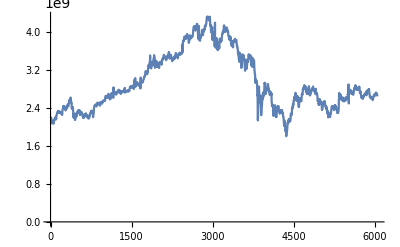

```mathematica
ListLinePlot[twapsWethUsdc90dFiltered6Week, PlotRange->All]
```

```mathematica
twapsWethUsdc90dFiltered8Week = Table[twapsWethUsdc90dFiltered[[i]], {i, 1, 8*6*24*7}]
```

{2.20799×10^9,2.20533×10^9,2.20572×10^9,2.20558×10^9,2.20476×10^9,2.2039×10^9,2.20513×10^9,2.2031×10^9,2.1997×10^9,2.1977×10^9,2.19642×10^9,2.19264×10^9,2.18452×10^9,2.17974×10^9,2.17409×10^9,2.16595×10^9,2.15763×10^9,2.14687×10^9,2.13229×10^9,2.11795×10^9,2.10658×10^9,2.10155×10^9,2.10459×10^9,2.10836×10^9,2.11006×10^9,2.10998×10^9,2.10671×10^9,2.09959×10^9,2.09156×10^9,2.08485×10^9,2.07922×10^9,2.07646×10^9,2.07685×10^9,2.08201×10^9,2.08605×10^9,2.0936×10^9,2.09635×10^9,2.10078×10^9,2.1063×10^9,2.11173×10^9,2.11541×10^9,2.12081×10^9,2.12707×10^9,2.13185×10^9,2.13614×10^9,2.13829×10^9,2.1356×10^9,2.13202×10^9,2.12948×10^9,2.12444×10^9,2.12109×10^9,2.11405×10^9,2.10656×10^9,2.09709×10^9,2.08876×10^9,2.08203×10^9,2.07571×10^9,2.076×10^9,2.07804×10^9,2.0826×10^9,2.092×10^9,2.10137×10^9,2.11342×10^9,2.12133×10^9,2.133×10^9,2.13803×10^9,2.14019×10^9,2.14584×10^9,2.14715×10^9,2.14686×10^9,2.14686×10^9,2.14853×10^9,2.15282×10^9,2.15936×10^9,2.16644×10^9,2.17366×10^9,2.18035×10^9,2.18508×10^9,2.18679×10^9,2.18661×10^9,2.18817×10^9,2.18892×10^9,2.18838×10^9,2.18555×10^9,2.18398×10^9,2.18084×10^9,2.17902×10^9,2.1791×10^9,2.18103×10^9,2.18514×10^9,2.19238×10^9,2.1997×10^9,2.20797×10^9,2.21494×10^9,2.21708×10^9,2.21531×10^9,2.20923×10^9,2.20054×10^9,2.19002×10^9,2.1798×10^9,2.17015×10^9,2.16504×10^9,2.16313×10^9,2.16575×10^9,2.17722×10^9,2.18669×10^9,2.20064×10^9,2.21318×10^9,2.2252×10^9,2.23608×10^9,2.24299×10^9,2.25221×10^9,2.25492×10^9,2.25937×10^9,2.2656×10^9,2.26918×10^9,2.27751×10^9,2.28222×10^9,2.28527×10^9,2.28614×10^9,2.28598×10^9,2.28635×10^9,2.29055×10^9,2.29529×10^9,2.30221×10^9,2.30863×10^9,2.31448×10^9,2.31796×10^9,2.31814×10^9,2.31637×10^9,2.31586×10^9,2.3173×10^9,2.31787×10^9,2.32308×10^9,2.32914×10^9,2.33406×10^9,2.33557×10^9,2.3385×10^9,2.33849×10^9,2.33491×10^9,2.33032×10^9,2.32851×10^9,2.32627×10^9,2.32693×10^9,2.327×10^9,2.32861×10^9,2.32872×10^9,2.3323×10^9,2.33609×10^9,2.34017×10^9,2.34079×10^9,2.33792×10^9,2.32664×10^9,2.31713×10^9,2.30791×10^9,2.30481×10^9,2.30593×10^9,2.31122×10^9,2.31633×10^9,2.31671×10^9,2.31654×10^9,2.31869×10^9,2.31917×10^9,2.32151×10^9,2.32353×10^9,2.32558×10^9,2.32512×10^9,2.32216×10^9,2.31566×10^9,2.30797×10^9,2.30158×10^9,2.30019×10^9,2.29582×10^9,2.29745×10^9,2.29969×10^9,2.3025×10^9,2.30329×10^9,2.30422×10^9,2.30287×10^9,2.3013×10^9,2.30039×10^9,2.30185×10^9,2.30393×10^9,2.30631×10^9,2.31256×10^9,2.31628×10^9,2.31432×10^9,2.31156×10^9,2.30752×10^9,2.30176×10^9,2.29729×10^9,2.29414×10^9,2.2911×10^9,2.28937×10^9,2.28748×10^9,2.28608×10^9,2.2887×10^9,2.29112×10^9,2.29267×10^9,2.29639×10^9,2.29873×10^9,2.30062×10^9,2.30202×10^9,2.3014×10^9,2.29931×10^9,2.29393×10^9,2.28801×10^9,2.28086×10^9,2.27559×10^9,2.27101×10^9,2.26585×10^9,2.26218×10^9,2.25884×10^9,2.25879×10^9,2.26032×10^9,2.27399×10^9,2.28924×10^9,2.31057×10^9,2.32906×10^9,2.35018×10^9,2.35935×10^9,2.36454×10^9,2.36951×10^9,2.37057×10^9,2.37302×10^9,2.37608×10^9,2.37666×10^9,2.37942×10^9,2.38804×10^9,2.3999×10^9,2.41264×10^9,2.42281×10^9,2.43272×10^9,2.43379×10^9,2.43288×10^9,2.43142×10^9,2.43641×10^9,2.44261×10^9,2.44738×10^9,2.44744×10^9,2.44522×10^9,2.43939×10^9,2.43497×10^9,2.43264×10^9,2.42861×10^9,2.42458×10^9,2.42349×10^9,2.42339×10^9,2.42106×10^9,2.41978×10^9,2.41792×10^9,2.41518×10^9,2.41306×10^9,2.41496×10^9,2.42005×10^9,2.42622×10^9,2.43092×10^9,2.43237×10^9,2.43004×10^9,2.42582×10^9,2.42046×10^9,2.41259×10^9,2.40775×10^9,2.40375×10^9,2.39108×10^9,2.39655×10^9,2.3956×10^9,2.39224×10^9,2.38944×10^9,2.39842×10^9,2.38836×10^9,2.38184×10^9,2.3781×10^9,2.3728×10^9,2.36321×10^9,2.35704×10^9,2.35824×10^9,2.36068×10^9,2.3603×10^9,2.36015×10^9,2.3579×10^9,2.35752×10^9,2.35909×10^9,2.36502×10^9,2.37908×10^9,2.39834×10^9,2.4127×10^9,2.42598×10^9,2.43401×10^9,2.43222×10^9,2.41886×10^9,2.40246×10^9,2.39316×10^9,2.38761×10^9,2.38868×10^9,2.40099×10^9,2.41134×10^9,2.41463×10^9,2.41221×10^9,2.40891×10^9,2.40558×10^9,2.40312×10^9,2.40413×10^9,2.41017×10^9,2.41718×10^9,2.4245×10^9,2.43149×10^9,2.43396×10^9,2.43713×10^9,2.43943×10^9,2.44341×10^9,2.45213×10^9,2.45836×10^9,2.47155×10^9,2.47967×10^9,2.48092×10^9,2.48045×10^9,2.47832×10^9,2.47252×10^9,2.46923×10^9,2.46871×10^9,2.46728×10^9,2.46567×10^9,2.46427×10^9,2.45963×10^9,2.45423×10^9,2.44689×10^9,2.44154×10^9,2.43926×10^9,2.44175×10^9,2.44538×10^9,2.45511×10^9,2.46241×10^9,2.47271×10^9,2.47959×10^9,2.48489×10^9,2.48836×10^9,2.49389×10^9,2.49936×10^9,2.50627×10^9,2.51533×10^9,2.52654×10^9,2.53708×10^9,2.54547×10^9,2.55359×10^9,2.56074×10^9,2.5665×10^9,2.57023×10^9,2.57431×10^9,2.57599×10^9,2.57284×10^9,2.57025×10^9,2.56978×10^9,2.56996×10^9,2.56804×10^9,2.56612×10^9,2.56696×10^9,2.56592×10^9,2.56733×10^9,2.57437×10^9,2.58211×10^9,2.58779×10^9,2.59054×10^9,2.59214×10^9,2.59185×10^9,2.59371×10^9,2.59943×10^9,2.60624×10^9,2.61565×10^9,2.6257×10^9,2.62317×10^9,2.61751×10^9,2.60893×10^9,2.59826×10^9,2.56573×10^9,2.55281×10^9,2.54389×10^9,2.54209×10^9,2.54473×10^9,2.54821×10^9,2.54514×10^9,2.53653×10^9,2.52562×10^9,2.51813×10^9,2.5154×10^9,2.51558×10^9,2.51916×10^9,2.51323×10^9,2.49936×10^9,2.48124×10^9,2.45851×10^9,2.42959×10^9,2.40366×10^9,2.39405×10^9,2.38788×10^9,2.38704×10^9,2.39695×10^9,2.41192×10^9,2.41702×10^9,2.41739×10^9,2.4192×10^9,2.41777×10^9,2.4136×10^9,2.41326×10^9,2.4183×10^9,2.42198×10^9,2.42571×10^9,2.42369×10^9,2.41881×10^9,2.41632×10^9,2.417×10^9,2.41421×10^9,2.41041×10^9,2.40525×10^9,2.39325×10^9,2.3742×10^9,2.35997×10^9,2.34364×10^9,2.33289×10^9,2.31322×10^9,2.28152×10^9,2.25267×10^9,2.2342×10^9,2.21876×10^9,2.21877×10^9,2.20542×10^9,2.24012×10^9,2.25011×10^9,2.25639×10^9,2.26274×10^9,2.28594×10^9,2.25998×10^9,2.25792×10^9,2.24987×10^9,2.23585×10^9,2.23095×10^9,2.21622×10^9,2.20627×10^9,2.20518×10^9,2.20774×10^9,2.20858×10^9,2.21536×10^9,2.21222×10^9,2.201×10^9,2.19372×10^9,2.18937×10^9,2.1898×10^9,2.19679×10^9,2.19911×10^9,2.1922×10^9,2.1814×10^9,2.16775×10^9,2.15329×10^9,2.14905×10^9,2.15453×10^9,2.16311×10^9,2.17754×10^9,2.1886×10^9,2.19496×10^9,2.19521×10^9,2.19642×10^9,2.19586×10^9,2.20198×10^9,2.21422×10^9,2.22915×10^9,2.24864×10^9,2.26186×10^9,2.26818×10^9,2.27401×10^9,2.27947×10^9,2.28488×10^9,2.28763×10^9,2.29374×10^9,2.2935×10^9,2.28949×10^9,2.28122×10^9,2.27718×10^9,2.26861×10^9,2.26267×10^9,2.25558×10^9,2.24668×10^9,2.23444×10^9,2.22963×10^9,2.22708×10^9,2.23103×10^9,2.2414×10^9,2.25694×10^9,2.26796×10^9,2.27638×10^9,2.28157×10^9,2.28064×10^9,2.28194×10^9,2.28855×10^9,2.29747×10^9,2.30827×10^9,2.32178×10^9,2.32668×10^9,2.33208×10^9,2.33238×10^9,2.3302×10^9,2.32706×10^9,2.32483×10^9,2.31294×10^9,2.30725×10^9,2.30586×10^9,2.30549×10^9,2.30875×10^9,2.32069×10^9,2.3289×10^9,2.33887×10^9,2.34455×10^9,2.34705×10^9,2.34831×10^9,2.34906×10^9,2.35316×10^9,2.35714×10^9,2.35986×10^9,2.36222×10^9,2.3601×10^9,2.3539×10^9,2.34852×10^9,2.34723×10^9,2.34445×10^9,2.34153×10^9,2.33929×10^9,2.33339×10^9,2.32678×10^9,2.32081×10^9,2.31699×10^9,2.31726×10^9,2.32052×10^9,2.32377×10^9,2.32889×10^9,2.33394×10^9,2.33811×10^9,2.34591×10^9,2.35097×10^9,2.3484×10^9,2.35168×10^9,2.32961×10^9,2.31129×10^9,2.29316×10^9,2.28242×10^9,2.26549×10^9,2.27423×10^9,2.27616×10^9,2.27699×10^9,2.27214×10^9,2.26531×10^9,2.26117×10^9,2.26262×10^9,2.26374×10^9,2.27259×10^9,2.28756×10^9,2.29605×10^9,2.30558×10^9,2.31085×10^9,2.31211×10^9,2.30824×10^9,2.30791×10^9,2.30698×10^9,2.30738×10^9,2.30927×10^9,2.31281×10^9,2.31167×10^9,2.31119×10^9,2.31043×10^9,2.31036×10^9,2.31235×10^9,2.31484×10^9,2.31729×10^9,2.31702×10^9,2.31256×10^9,2.30616×10^9,2.30047×10^9,2.29057×10^9,2.28115×10^9,2.27844×10^9,2.27622×10^9,2.27517×10^9,2.27651×10^9,2.28024×10^9,2.2841×10^9,2.28743×10^9,2.29157×10^9,2.29036×10^9,2.28662×10^9,2.2796×10^9,2.27321×10^9,2.26679×10^9,2.26409×10^9,2.25823×10^9,2.25215×10^9,2.24222×10^9,2.2328×10^9,2.22194×10^9,2.21341×10^9,2.20809×10^9,2.20552×10^9,2.20414×10^9,2.19895×10^9,2.19647×10^9,2.19691×10^9,2.19647×10^9,2.19503×10^9,2.20427×10^9,2.21535×10^9,2.2193×10^9,2.22389×10^9,2.22751×10^9,2.22651×10^9,2.22377×10^9,2.22182×10^9,2.21675×10^9,2.21353×10^9,2.2085×10^9,2.2066×10^9,2.2045×10^9,2.20086×10^9,2.20024×10^9,2.20296×10^9,2.2091×10^9,2.21676×10^9,2.23307×10^9,2.24249×10^9,2.24753×10^9,2.25021×10^9,2.24966×10^9,2.24755×10^9,2.2456×10^9,2.23852×10^9,2.23414×10^9,2.2323×10^9,2.23331×10^9,2.23724×10^9,2.25193×10^9,2.26192×10^9,2.2681×10^9,2.27309×10^9,2.27821×10^9,2.27709×10^9,2.27605×10^9,2.2762×10^9,2.27657×10^9,2.2759×10^9,2.27331×10^9,2.27229×10^9,2.27357×10^9,2.27615×10^9,2.27991×10^9,2.28524×10^9,2.28907×10^9,2.28996×10^9,2.28935×10^9,2.28902×10^9,2.28737×10^9,2.28427×10^9,2.28126×10^9,2.27787×10^9,2.2695×10^9,2.2637×10^9,2.25955×10^9,2.25705×10^9,2.25289×10^9,2.24485×10^9,2.23883×10^9,2.23579×10^9,2.23314×10^9,2.22735×10^9,2.22636×10^9,2.22483×10^9,2.22245×10^9,2.2202×10^9,2.22366×10^9,2.22793×10^9,2.23311×10^9,2.23822×10^9,2.24126×10^9,2.2419×10^9,2.2428×10^9,2.2431×10^9,2.24391×10^9,2.24438×10^9,2.24251×10^9,2.23764×10^9,2.23285×10^9,2.22346×10^9,2.21278×10^9,2.20363×10^9,2.19764×10^9,2.19271×10^9,2.18978×10^9,2.18801×10^9,2.18846×10^9,2.18976×10^9,2.19189×10^9,2.19508×10^9,2.19872×10^9,2.19979×10^9,2.20061×10^9,2.20091×10^9,2.20067×10^9,2.20039×10^9,2.19911×10^9,2.19718×10^9,2.19265×10^9,2.18857×10^9,2.18462×10^9,2.18244×10^9,2.18365×10^9,2.18494×10^9,2.18744×10^9,2.19216×10^9,2.19477×10^9,2.20087×10^9,2.20936×10^9,2.21653×10^9,2.22071×10^9,2.2223×10^9,2.2192×10^9,2.22228×10^9,2.22865×10^9,2.23954×10^9,2.25415×10^9,2.26709×10^9,2.27141×10^9,2.27257×10^9,2.26885×10^9,2.26645×10^9,2.26725×10^9,2.26852×10^9,2.27247×10^9,2.27791×10^9,2.28419×10^9,2.29287×10^9,2.29906×10^9,2.30388×10^9,2.30929×10^9,2.31112×10^9,2.31317×10^9,2.31564×10^9,2.31573×10^9,2.31561×10^9,2.31542×10^9,2.31413×10^9,2.31519×10^9,2.31908×10^9,2.32147×10^9,2.32736×10^9,2.33494×10^9,2.33998×10^9,2.34386×10^9,2.34424×10^9,2.34487×10^9,2.34497×10^9,2.34218×10^9,2.34076×10^9,2.3418×10^9,2.34242×10^9,2.34246×10^9,2.34516×10^9,2.34479×10^9,2.34044×10^9,2.33679×10^9,2.33343×10^9,2.3292×10^9,2.32519×10^9,2.32298×10^9,2.31663×10^9,2.30992×10^9,2.3041×10^9,2.29961×10^9,2.29866×10^9,2.29799×10^9,2.29939×10^9,2.2985×10^9,2.29236×10^9,2.28655×10^9,2.28392×10^9,2.2809×10^9,2.27635×10^9,2.26595×10^9,2.25331×10^9,2.24366×10^9,2.22887×10^9,2.2145×10^9,2.21107×10^9,2.21254×10^9,2.21443×10^9,2.22275×10^9,2.23622×10^9,2.24861×10^9,2.2594×10^9,2.26408×10^9,2.27033×10^9,2.2803×10^9,2.28652×10^9,2.29094×10^9,2.2981×10^9,2.31555×10^9,2.3368×10^9,2.35786×10^9,2.3769×10^9,2.39538×10^9,2.40696×10^9,2.41176×10^9,2.41569×10^9,2.42174×10^9,2.42885×10^9,2.4366×10^9,2.44476×10^9,2.44712×10^9,2.44617×10^9,2.44403×10^9,2.44363×10^9,2.44219×10^9,2.44623×10^9,2.44958×10^9,2.45123×10^9,2.45112×10^9,2.45167×10^9,2.45407×10^9,2.45812×10^9,2.46162×10^9,2.46369×10^9,2.46427×10^9,2.46289×10^9,2.45751×10^9,2.45375×10^9,2.45255×10^9,2.4526×10^9,2.45302×10^9,2.45883×10^9,2.46523×10^9,2.47045×10^9,2.47648×10^9,2.48128×10^9,2.48101×10^9,2.47698×10^9,2.47104×10^9,2.46507×10^9,2.46046×10^9,2.45761×10^9,2.45548×10^9,2.45276×10^9,2.44984×10^9,2.44595×10^9,2.44291×10^9,2.44226×10^9,2.44154×10^9,2.43928×10^9,2.43783×10^9,2.44323×10^9,2.45125×10^9,2.45873×10^9,2.47179×10^9,2.48318×10^9,2.48587×10^9,2.48714×10^9,2.48866×10^9,2.49182×10^9,2.49573×10^9,2.50131×10^9,2.50888×10^9,2.51503×10^9,2.51715×10^9,2.51551×10^9,2.5143×10^9,2.51203×10^9,2.50693×10^9,2.50391×10^9,2.49954×10^9,2.49506×10^9,2.49414×10^9,2.49543×10^9,2.49693×10^9,2.4989×10^9,2.49877×10^9,2.49364×10^9,2.49147×10^9,2.48988×10^9,2.48811×10^9,2.48799×10^9,2.48933×10^9,2.49132×10^9,2.49484×10^9,2.49545×10^9,2.49487×10^9,2.48933×10^9,2.48526×10^9,2.48001×10^9,2.48286×10^9,2.49015×10^9,2.50192×10^9,2.50791×10^9,2.51492×10^9,2.51568×10^9,2.51417×10^9,2.50893×10^9,2.50468×10^9,2.50156×10^9,2.49831×10^9,2.49638×10^9,2.49477×10^9,2.49335×10^9,2.49183×10^9,2.49079×10^9,2.48908×10^9,2.48649×10^9,2.48389×10^9,2.48105×10^9,2.47142×10^9,2.46433×10^9,2.45583×10^9,2.45223×10^9,2.45422×10^9,2.46197×10^9,2.47306×10^9,2.4924×10^9,2.50467×10^9,2.51184×10^9,2.51584×10^9,2.51972×10^9,2.51729×10^9,2.51696×10^9,2.51681×10^9,2.51826×10^9,2.52155×10^9,2.52454×10^9,2.52341×10^9,2.52264×10^9,2.52008×10^9,2.51702×10^9,2.51238×10^9,2.51208×10^9,2.51191×10^9,2.51242×10^9,2.51245×10^9,2.5126×10^9,2.51481×10^9,2.51713×10^9,2.51884×10^9,2.52143×10^9,2.5239×10^9,2.52503×10^9,2.52365×10^9,2.51914×10^9,2.51419×10^9,2.50823×10^9,2.50277×10^9,2.49839×10^9,2.49751×10^9,2.49796×10^9,2.49829×10^9,2.49901×10^9,2.50106×10^9,2.50468×10^9,2.50984×10^9,2.51568×10^9,2.52184×10^9,2.52488×10^9,2.52826×10^9,2.53554×10^9,2.53955×10^9,2.54475×10^9,2.54931×10^9,2.55421×10^9,2.55606×10^9,2.55704×10^9,2.558×10^9,2.55742×10^9,2.55613×10^9,2.55383×10^9,2.55188×10^9,2.55033×10^9,2.55004×10^9,2.54953×10^9,2.54977×10^9,2.54832×10^9,2.54754×10^9,2.547×10^9,2.54779×10^9,2.54815×10^9,2.5505×10^9,2.55165×10^9,2.55143×10^9,2.55092×10^9,2.55027×10^9,2.54893×10^9,2.54858×10^9,2.55059×10^9,2.553×10^9,2.55592×10^9,2.55994×10^9,2.56424×10^9,2.56771×10^9,2.57182×10^9,2.57375×10^9,2.57396×10^9,2.57164×10^9,2.56896×10^9,2.56596×10^9,2.5636×10^9,2.56107×10^9,2.55891×10^9,2.5563×10^9,2.55368×10^9,2.55618×10^9,2.56814×10^9,2.57934×10^9,2.59744×10^9,2.61451×10^9,2.62719×10^9,2.63082×10^9,2.6356×10^9,2.64104×10^9,2.64795×10^9,2.65163×10^9,2.65855×10^9,2.65906×10^9,2.65748×10^9,2.65239×10^9,2.65007×10^9,2.64537×10^9,2.6422×10^9,2.63909×10^9,2.63922×10^9,2.63904×10^9,2.63858×10^9,2.63735×10^9,2.63764×10^9,2.63803×10^9,2.63722×10^9,2.63794×10^9,2.6394×10^9,2.63626×10^9,2.6309×10^9,2.62599×10^9,2.62427×10^9,2.62282×10^9,2.62459×10^9,2.62923×10^9,2.63363×10^9,2.63453×10^9,2.63619×10^9,2.63742×10^9,2.6365×10^9,2.63813×10^9,2.63956×10^9,2.63923×10^9,2.63813×10^9,2.63675×10^9,2.63277×10^9,2.62774×10^9,2.6252×10^9,2.62523×10^9,2.62802×10^9,2.63213×10^9,2.63998×10^9,2.65069×10^9,2.66276×10^9,2.67138×10^9,2.67884×10^9,2.6839×10^9,2.68591×10^9,2.68649×10^9,2.68838×10^9,2.69162×10^9,2.69579×10^9,2.69895×10^9,2.70219×10^9,2.70203×10^9,2.6985×10^9,2.69107×10^9,2.68116×10^9,2.6707×10^9,2.65959×10^9,2.65079×10^9,2.6437×10^9,2.64043×10^9,2.63928×10^9,2.63988×10^9,2.6411×10^9,2.64281×10^9,2.6419×10^9,2.63996×10^9,2.63913×10^9,2.63692×10^9,2.63059×10^9,2.629×10^9,2.62375×10^9,2.6125×10^9,2.6043×10^9,2.59472×10^9,2.59248×10^9,2.58477×10^9,2.58679×10^9,2.59057×10^9,2.5975×10^9,2.60157×10^9,2.60817×10^9,2.61214×10^9,2.61509×10^9,2.61697×10^9,2.61809×10^9,2.61915×10^9,2.61857×10^9,2.61463×10^9,2.60977×10^9,2.60421×10^9,2.6001×10^9,2.60019×10^9,2.60194×10^9,2.60676×10^9,2.61245×10^9,2.61714×10^9,2.62146×10^9,2.62891×10^9,2.63716×10^9,2.64614×10^9,2.65821×10^9,2.67367×10^9,2.68377×10^9,2.69346×10^9,2.70188×10^9,2.70791×10^9,2.71172×10^9,2.71441×10^9,2.71902×10^9,2.71242×10^9,2.70675×10^9,2.70174×10^9,2.69608×10^9,2.69353×10^9,2.69857×10^9,2.7032×10^9,2.70851×10^9,2.71255×10^9,2.71347×10^9,2.71033×10^9,2.70519×10^9,2.69555×10^9,2.68986×10^9,2.68374×10^9,2.68337×10^9,2.68503×10^9,2.68906×10^9,2.69365×10^9,2.70085×10^9,2.7055×10^9,2.71066×10^9,2.71477×10^9,2.71774×10^9,2.71978×10^9,2.71976×10^9,2.71957×10^9,2.72293×10^9,2.72605×10^9,2.72826×10^9,2.61748×10^9,2.72971×10^9,2.72785×10^9,2.72473×10^9,2.72449×10^9,2.83875×10^9,2.73048×10^9,2.70685×10^9,2.72574×10^9,2.72363×10^9,2.71831×10^9,2.71326×10^9,2.73625×10^9,2.71169×10^9,2.71164×10^9,2.71516×10^9,2.72376×10^9,2.73414×10^9,2.74182×10^9,2.74377×10^9,2.74286×10^9,2.73679×10^9,2.72737×10^9,2.72313×10^9,2.72223×10^9,2.72211×10^9,2.72412×10^9,2.73119×10^9,2.73578×10^9,2.73961×10^9,2.74275×10^9,2.74377×10^9,2.74148×10^9,2.73802×10^9,2.73215×10^9,2.72686×10^9,2.72274×10^9,2.71851×10^9,2.71589×10^9,2.71682×10^9,2.71852×10^9,2.71973×10^9,2.72099×10^9,2.72118×10^9,2.72036×10^9,2.71803×10^9,2.71711×10^9,2.71625×10^9,2.71402×10^9,2.7077×10^9,2.70253×10^9,2.69641×10^9,2.69104×10^9,2.68881×10^9,2.6873×10^9,2.68706×10^9,2.68928×10^9,2.69198×10^9,2.69406×10^9,2.69883×10^9,2.70389×10^9,2.70778×10^9,2.71183×10^9,2.71527×10^9,2.72096×10^9,2.72397×10^9,2.72755×10^9,2.72925×10^9,2.72992×10^9,2.73064×10^9,2.73154×10^9,2.73126×10^9,2.73096×10^9,2.7294×10^9,2.72633×10^9,2.724×10^9,2.72102×10^9,2.71824×10^9,2.72097×10^9,2.72841×10^9,2.73666×10^9,2.74697×10^9,2.75731×10^9,2.7641×10^9,2.76504×10^9,2.76546×10^9,2.76513×10^9,2.76459×10^9,2.76491×10^9,2.76668×10^9,2.76743×10^9,2.76769×10^9,2.76806×10^9,2.76717×10^9,2.76543×10^9,2.76721×10^9,2.77086×10^9,2.775×10^9,2.78064×10^9,2.78663×10^9,2.78752×10^9,2.78625×10^9,2.78341×10^9,2.77901×10^9,2.77219×10^9,2.76783×10^9,2.76488×10^9,2.76346×10^9,2.7638×10^9,2.76513×10^9,2.7666×10^9,2.76932×10^9,2.77417×10^9,2.77752×10^9,2.78108×10^9,2.7845×10^9,2.78344×10^9,2.77817×10^9,2.77243×10^9,2.76555×10^9,2.75762×10^9,2.74739×10^9,2.74127×10^9,2.738×10^9,2.7346×10^9,2.73519×10^9,2.73259×10^9,2.72757×10^9,2.72235×10^9,2.7184×10^9,2.71327×10^9,2.71615×10^9,2.71967×10^9,2.72248×10^9,2.72501×10^9,2.72742×10^9,2.72738×10^9,2.72296×10^9,2.71582×10^9,2.71306×10^9,2.71057×10^9,2.70641×10^9,2.70649×10^9,2.70927×10^9,2.7094×10^9,2.70879×10^9,2.71196×10^9,2.71795×10^9,2.72507×10^9,2.73315×10^9,2.74055×10^9,2.74832×10^9,2.7532×10^9,2.75747×10^9,2.76008×10^9,2.76143×10^9,2.76196×10^9,2.76191×10^9,2.76149×10^9,2.75977×10^9,2.7548×10^9,2.75368×10^9,2.75089×10^9,2.7477×10^9,2.74435×10^9,2.74318×10^9,2.73905×10^9,2.73823×10^9,2.73931×10^9,2.74195×10^9,2.74371×10^9,2.74567×10^9,2.74399×10^9,2.74219×10^9,2.7421×10^9,2.74112×10^9,2.74029×10^9,2.74087×10^9,2.74219×10^9,2.74109×10^9,2.7422×10^9,2.74414×10^9,2.74721×10^9,2.75003×10^9,2.75336×10^9,2.75674×10^9,2.75873×10^9,2.76045×10^9,2.76198×10^9,2.7632×10^9,2.76403×10^9,2.76461×10^9,2.76565×10^9,2.76728×10^9,2.77046×10^9,2.77379×10^9,2.77742×10^9,2.78123×10^9,2.78293×10^9,2.7827×10^9,2.78245×10^9,2.78097×10^9,2.77977×10^9,2.77746×10^9,2.77616×10^9,2.77466×10^9,2.77401×10^9,2.77533×10^9,2.7787×10^9,2.78216×10^9,2.80134×10^9,2.78906×10^9,2.78842×10^9,2.78723×10^9,2.82806×10^9,2.76798×10^9,2.78159×10^9,2.7813×10^9,2.77825×10^9,2.72922×10^9,2.76753×10^9,2.76317×10^9,2.75753×10^9,2.75353×10^9,2.75102×10^9,2.7483×10^9,2.74567×10^9,2.74392×10^9,2.74468×10^9,2.74638×10^9,2.74819×10^9,2.7477×10^9,2.74719×10^9,2.74595×10^9,2.74403×10^9,2.74128×10^9,2.74355×10^9,2.74612×10^9,2.7494×10^9,2.75331×10^9,2.75533×10^9,2.75248×10^9,2.7507×10^9,2.74822×10^9,2.74593×10^9,2.7459×10^9,2.74559×10^9,2.74579×10^9,2.74671×10^9,2.74729×10^9,2.7484×10^9,2.75239×10^9,2.75614×10^9,2.75919×10^9,2.76152×10^9,2.7637×10^9,2.76366×10^9,2.76471×10^9,2.76466×10^9,2.76468×10^9,2.76518×10^9,2.76498×10^9,2.76413×10^9,2.76529×10^9,2.76855×10^9,2.77194×10^9,2.77473×10^9,2.77689×10^9,2.77822×10^9,2.77799×10^9,2.77618×10^9,2.77409×10^9,2.77224×10^9,2.76982×10^9,2.76719×10^9,2.7649×10^9,2.7613×10^9,2.75929×10^9,2.75776×10^9,2.75645×10^9,2.75597×10^9,2.75652×10^9,2.75541×10^9,2.7544×10^9,2.75292×10^9,2.75267×10^9,2.75227×10^9,2.7536×10^9,2.75607×10^9,2.75943×10^9,2.76309×10^9,2.76715×10^9,2.76933×10^9,2.77048×10^9,2.77078×10^9,2.77071×10^9,2.76979×10^9,2.76909×10^9,2.76776×10^9,2.76768×10^9,2.76883×10^9,2.77949×10^9,2.79242×10^9,2.80527×10^9,2.81563×10^9,2.82967×10^9,2.83186×10^9,2.83186×10^9,2.83116×10^9,2.83322×10^9,2.83502×10^9,2.83731×10^9,2.8405×10^9,2.84328×10^9,2.84375×10^9,2.84361×10^9,2.84323×10^9,2.84274×10^9,2.84259×10^9,2.84563×10^9,2.85031×10^9,2.85527×10^9,2.85864×10^9,2.86233×10^9,2.86076×10^9,2.85856×10^9,2.85557×10^9,2.85439×10^9,2.85513×10^9,2.85625×10^9,2.85655×10^9,2.85682×10^9,2.85649×10^9,2.85557×10^9,2.85521×10^9,2.85615×10^9,2.85757×10^9,2.85818×10^9,2.8577×10^9,2.85372×10^9,2.84594×10^9,2.83934×10^9,2.83444×10^9,2.8325×10^9,2.83316×10^9,2.83598×10^9,2.8374×10^9,2.83687×10^9,2.83468×10^9,2.83461×10^9,2.83743×10^9,2.84098×10^9,2.84543×10^9,2.84947×10^9,2.8527×10^9,2.854×10^9,2.8552×10^9,2.85894×10^9,2.8634×10^9,2.86716×10^9,2.87105×10^9,2.87345×10^9,2.87385×10^9,2.87273×10^9,2.87143×10^9,2.86996×10^9,2.86907×10^9,2.86878×10^9,2.86857×10^9,2.86782×10^9,2.86742×10^9,2.86603×10^9,2.8637×10^9,2.86046×10^9,2.85818×10^9,2.85434×10^9,2.8527×10^9,2.85328×10^9,2.85804×10^9,2.86276×10^9,2.86969×10^9,2.87547×10^9,2.80645×10^9,2.88817×10^9,2.89516×10^9,2.90277×10^9,2.90995×10^9,2.99492×10^9,2.92215×10^9,2.92512×10^9,2.9281×10^9,2.93023×10^9,2.93112×10^9,2.9317×10^9,2.93274×10^9,2.93337×10^9,2.93337×10^9,2.93266×10^9,2.92963×10^9,2.92575×10^9,2.92503×10^9,2.92361×10^9,2.9247×10^9,2.9292×10^9,2.93421×10^9,2.93769×10^9,3.03478×10^9,2.93804×10^9,2.93441×10^9,2.93127×10^9,2.92849×10^9,2.84973×10^9,2.9289×10^9,2.93166×10^9,2.93378×10^9,2.93654×10^9,2.93757×10^9,2.93919×10^9,2.94188×10^9,2.94373×10^9,2.94649×10^9,2.94615×10^9,2.94533×10^9,2.94334×10^9,2.9416×10^9,2.93936×10^9,2.93819×10^9,2.93651×10^9,2.93576×10^9,2.93568×10^9,2.93596×10^9,2.93709×10^9,2.93933×10^9,2.94297×10^9,2.94542×10^9,2.94764×10^9,2.94994×10^9,2.95137×10^9,2.9515×10^9,2.95024×10^9,2.94409×10^9,2.93685×10^9,2.92533×10^9,2.91281×10^9,2.91113×10^9,2.91184×10^9,2.91191×10^9,2.91431×10^9,2.91738×10^9,2.91731×10^9,2.91522×10^9,2.91575×10^9,2.91633×10^9,2.9172×10^9,2.91769×10^9,2.91803×10^9,2.91747×10^9,2.91558×10^9,2.90994×10^9,2.90433×10^9,2.89991×10^9,2.89507×10^9,2.89195×10^9,2.88844×10^9,2.88498×10^9,2.87998×10^9,2.87532×10^9,2.87316×10^9,2.87376×10^9,2.875×10^9,2.87711×10^9,2.87898×10^9,2.88206×10^9,2.88564×10^9,2.89221×10^9,2.89905×10^9,2.90687×10^9,2.91168×10^9,2.9154×10^9,2.91581×10^9,2.91519×10^9,2.91474×10^9,2.91469×10^9,2.91541×10^9,2.91761×10^9,2.9211×10^9,2.92439×10^9,2.92719×10^9,2.92829×10^9,2.92738×10^9,2.92673×10^9,2.92583×10^9,2.92599×10^9,2.92453×10^9,2.92212×10^9,2.92077×10^9,2.91849×10^9,2.9166×10^9,2.9168×10^9,2.91798×10^9,2.91889×10^9,2.91928×10^9,2.91902×10^9,2.81586×10^9,2.91997×10^9,2.92207×10^9,2.92466×10^9,2.92757×10^9,3.04472×10^9,2.93313×10^9,2.93374×10^9,2.93474×10^9,2.93518×10^9,2.93494×10^9,2.93477×10^9,2.93473×10^9,2.93493×10^9,2.93632×10^9,2.938×10^9,2.94001×10^9,2.94144×10^9,2.94487×10^9,2.94892×10^9,2.95266×10^9,2.9592×10^9,2.96545×10^9,2.96951×10^9,2.97281×10^9,2.97447×10^9,2.97448×10^9,2.97352×10^9,2.97196×10^9,2.97037×10^9,2.96885×10^9,2.96757×10^9,2.96789×10^9,2.96959×10^9,2.97161×10^9,2.97374×10^9,2.97396×10^9,2.97038×10^9,2.96509×10^9,2.95729×10^9,2.94817×10^9,2.94357×10^9,2.94192×10^9,2.94294×10^9,2.94426×10^9,2.94644×10^9,2.95175×10^9,2.95794×10^9,2.96718×10^9,2.97438×10^9,2.98319×10^9,2.98637×10^9,2.98854×10^9,2.99013×10^9,2.99205×10^9,2.99826×10^9,3.00421×10^9,3.00858×10^9,3.01404×10^9,3.01764×10^9,3.01749×10^9,3.01875×10^9,3.02059×10^9,3.02486×10^9,3.02954×10^9,3.03463×10^9,3.03939×10^9,3.04473×10^9,3.04978×10^9,3.05285×10^9,3.0543×10^9,3.05471×10^9,3.0537×10^9,3.05238×10^9,3.05422×10^9,3.05571×10^9,3.06099×10^9,3.0702×10^9,3.08027×10^9,3.08642×10^9,3.08984×10^9,3.09292×10^9,3.09329×10^9,3.09247×10^9,3.09069×10^9,3.0893×10^9,3.09236×10^9,3.10229×10^9,3.11249×10^9,3.12166×10^9,3.13349×10^9,3.14192×10^9,3.14816×10^9,3.1563×10^9,3.16645×10^9,3.17416×10^9,3.17874×10^9,3.1755×10^9,3.17232×10^9,3.16874×10^9,3.16586×10^9,3.16861×10^9,3.16742×10^9,3.16414×10^9,3.1593×10^9,3.15435×10^9,3.14781×10^9,3.14722×10^9,3.14946×10^9,3.15466×10^9,3.15986×10^9,3.16539×10^9,3.16726×10^9,3.16749×10^9,3.16459×10^9,3.15916×10^9,3.1508×10^9,3.14581×10^9,3.14291×10^9,3.13797×10^9,3.13545×10^9,3.13475×10^9,3.12745×10^9,3.12068×10^9,3.11636×10^9,3.11706×10^9,3.11962×10^9,3.12807×10^9,3.14131×10^9,3.1519×10^9,3.15746×10^9,3.1652×10^9,3.17054×10^9,3.17034×10^9,3.17038×10^9,3.17194×10^9,3.17099×10^9,3.16982×10^9,3.17997×10^9,3.19805×10^9,3.21332×10^9,3.2328×10^9,3.25006×10^9,3.26408×10^9,3.26847×10^9,3.27346×10^9,3.28292×10^9,3.28874×10^9,3.29368×10^9,3.30162×10^9,3.30984×10^9,3.31551×10^9,3.31525×10^9,3.30975×10^9,3.30738×10^9,3.30371×10^9,3.29632×10^9,3.29271×10^9,3.2954×10^9,3.291×10^9,3.28432×10^9,3.28393×10^9,3.28365×10^9,3.28322×10^9,3.28341×10^9,3.28726×10^9,3.28674×10^9,3.29249×10^9,3.30197×10^9,3.32134×10^9,3.34054×10^9,3.35925×10^9,3.37253×10^9,3.38068×10^9,3.38782×10^9,3.39434×10^9,3.40513×10^9,3.41667×10^9,3.42637×10^9,3.51266×10^9,3.41029×10^9,3.39725×10^9,3.38664×10^9,3.35792×10^9,3.24986×10^9,3.32865×10^9,3.31206×10^9,3.29581×10^9,3.29777×10^9,3.30036×10^9,3.29862×10^9,3.28909×10^9,3.27985×10^9,3.27262×10^9,3.25998×10^9,3.24619×10^9,3.24303×10^9,3.24156×10^9,3.24031×10^9,3.24427×10^9,3.24642×10^9,3.24701×10^9,3.25556×10^9,3.26539×10^9,3.27686×10^9,3.29305×10^9,3.31134×10^9,3.32849×10^9,3.34022×10^9,3.35294×10^9,3.35822×10^9,3.36525×10^9,3.3693×10^9,3.37145×10^9,3.37457×10^9,3.37841×10^9,3.37754×10^9,3.37142×10^9,3.36896×10^9,3.36567×10^9,3.3615×10^9,3.35694×10^9,3.35295×10^9,3.34424×10^9,3.33067×10^9,3.32129×10^9,3.31551×10^9,3.30967×10^9,3.30488×10^9,3.31224×10^9,3.31948×10^9,3.33212×10^9,3.34441×10^9,3.35342×10^9,3.35429×10^9,3.35717×10^9,3.36256×10^9,3.36871×10^9,3.38226×10^9,3.39839×10^9,3.40725×10^9,3.41138×10^9,3.41839×10^9,3.42868×10^9,3.43749×10^9,3.44802×10^9,3.45623×10^9,3.45604×10^9,3.45006×10^9,3.45079×10^9,3.44972×10^9,3.45783×10^9,3.46868×10^9,3.51917×10^9,3.49037×10^9,3.48956×10^9,3.49155×10^9,3.48313×10^9,3.4358×10^9,3.43892×10^9,3.42236×10^9,3.39615×10^9,3.37087×10^9,3.34657×10^9,3.31593×10^9,3.29004×10^9,3.28075×10^9,3.27893×10^9,3.2681×10^9,3.25206×10^9,3.25651×10^9,3.26333×10^9,3.266×10^9,3.27289×10^9,3.29005×10^9,3.30333×10^9,3.30959×10^9,3.31795×10^9,3.3263×10^9,3.33685×10^9,3.34964×10^9,3.35788×10^9,3.36501×10^9,3.37315×10^9,3.38492×10^9,3.38066×10^9,3.3892×10^9,3.40191×10^9,3.40186×10^9,3.38829×10^9,3.39475×10^9,3.38859×10^9,3.38107×10^9,3.38142×10^9,3.38023×10^9,3.37093×10^9,3.36058×10^9,3.35022×10^9,3.33532×10^9,3.31576×10^9,3.30652×10^9,3.28881×10^9,3.28516×10^9,3.28866×10^9,3.29359×10^9,3.29752×10^9,3.29343×10^9,3.28286×10^9,3.2772×10^9,3.27467×10^9,3.27531×10^9,3.28842×10^9,3.30126×10^9,3.31071×10^9,3.3224×10^9,3.33405×10^9,3.34239×10^9,3.35175×10^9,3.36104×10^9,3.36×10^9,3.3598×10^9,3.35398×10^9,3.34512×10^9,3.33837×10^9,3.32631×10^9,3.31173×10^9,3.30417×10^9,3.29825×10^9,3.29722×10^9,3.29596×10^9,3.29762×10^9,3.3007×10^9,3.30004×10^9,3.29202×10^9,3.28085×10^9,3.27257×10^9,3.26674×10^9,3.26707×10^9,3.2698×10^9,3.27276×10^9,3.27289×10^9,3.26668×10^9,3.25799×10^9,3.25262×10^9,3.25011×10^9,3.25127×10^9,3.25661×10^9,3.26576×10^9,3.27656×10^9,3.29321×10^9,3.31361×10^9,3.32532×10^9,3.3378×10^9,3.34953×10^9,3.35215×10^9,3.35474×10^9,3.35306×10^9,3.35051×10^9,3.3493×10^9,3.35174×10^9,3.36157×10^9,3.37043×10^9,3.37489×10^9,3.3781×10^9,3.37729×10^9,3.37389×10^9,3.37052×10^9,3.36914×10^9,3.36728×10^9,3.36537×10^9,3.36126×10^9,3.35838×10^9,3.36096×10^9,3.36457×10^9,3.3672×10^9,3.3687×10^9,3.37161×10^9,3.37156×10^9,3.37133×10^9,3.37312×10^9,3.37377×10^9,3.37571×10^9,3.37184×10^9,3.36254×10^9,3.34794×10^9,3.33756×10^9,3.33144×10^9,3.3282×10^9,3.32911×10^9,3.33675×10^9,3.33777×10^9,3.33083×10^9,3.32658×10^9,3.32181×10^9,3.32384×10^9,3.33698×10^9,3.35683×10^9,3.37555×10^9,3.40635×10^9,3.42307×10^9,3.42605×10^9,3.42653×10^9,3.42208×10^9,3.41643×10^9,3.41196×10^9,3.41093×10^9,3.41133×10^9,3.41151×10^9,3.41222×10^9,3.41535×10^9,3.4203×10^9,3.42624×10^9,3.43622×10^9,3.44464×10^9,3.45552×10^9,3.46154×10^9,3.46323×10^9,3.46303×10^9,3.46052×10^9,3.45735×10^9,3.45413×10^9,3.45352×10^9,3.45198×10^9,3.4458×10^9,3.44212×10^9,3.43952×10^9,3.44475×10^9,3.4542×10^9,3.47486×10^9,3.48566×10^9,3.50763×10^9,3.5143×10^9,3.5187×10^9,3.52307×10^9,3.52401×10^9,3.52443×10^9,3.52302×10^9,3.51368×10^9,3.50429×10^9,3.49398×10^9,3.48502×10^9,3.47471×10^9,3.47133×10^9,3.46861×10^9,3.47011×10^9,3.47167×10^9,3.47457×10^9,3.47948×10^9,3.48454×10^9,3.48789×10^9,3.48886×10^9,3.4901×10^9,3.48767×10^9,3.48328×10^9,3.47816×10^9,3.47322×10^9,3.46939×10^9,3.47022×10^9,3.47472×10^9,3.47892×10^9,3.48229×10^9,3.48288×10^9,3.47733×10^9,3.46901×10^9,3.45886×10^9,3.45214×10^9,3.45047×10^9,3.4511×10^9,3.45088×10^9,3.45123×10^9,3.44522×10^9,3.43796×10^9,3.42941×10^9,3.42031×10^9,3.41839×10^9,3.41277×10^9,3.41588×10^9,3.42038×10^9,3.42859×10^9,3.43534×10^9,3.43857×10^9,3.44491×10^9,3.44685×10^9,3.44589×10^9,3.44467×10^9,3.44487×10^9,3.44461×10^9,3.44562×10^9,3.44888×10^9,3.4538×10^9,3.46161×10^9,3.46931×10^9,3.47585×10^9,3.48429×10^9,3.48798×10^9,3.48863×10^9,3.48842×10^9,3.49183×10^9,3.49581×10^9,3.50211×10^9,3.50543×10^9,3.50945×10^9,3.50871×10^9,3.50535×10^9,3.49845×10^9,3.49544×10^9,3.49064×10^9,3.48719×10^9,3.48625×10^9,3.48553×10^9,3.48357×10^9,3.48326×10^9,3.48508×10^9,3.48769×10^9,3.49314×10^9,3.50298×10^9,3.51713×10^9,3.53195×10^9,3.54276×10^9,3.552×10^9,3.56154×10^9,3.56924×10^9,3.57419×10^9,3.57553×10^9,3.57612×10^9,3.5747×10^9,3.57416×10^9,3.57271×10^9,3.57542×10^9,3.57985×10^9,3.57558×10^9,3.56714×10^9,3.55475×10^9,3.52847×10^9,3.506×10^9,3.48667×10^9,3.46469×10^9,3.44775×10^9,3.44929×10^9,3.45703×10^9,3.45856×10^9,3.46189×10^9,3.46556×10^9,3.46594×10^9,3.45981×10^9,3.46164×10^9,3.46529×10^9,3.47151×10^9,3.47804×10^9,3.48588×10^9,3.49797×10^9,3.50547×10^9,3.51189×10^9,3.51617×10^9,3.52243×10^9,3.52508×10^9,3.52548×10^9,3.52188×10^9,3.51816×10^9,3.51098×10^9,3.5064×10^9,3.49862×10^9,3.50178×10^9,3.50415×10^9,3.50526×10^9,3.50894×10^9,3.5134×10^9,3.5073×10^9,3.50054×10^9,3.49562×10^9,3.48685×10^9,3.47766×10^9,3.47324×10^9,3.47043×10^9,3.46536×10^9,3.45702×10^9,3.4508×10^9,3.44617×10^9,3.44086×10^9,3.43222×10^9,3.43008×10^9,3.42999×10^9,3.43042×10^9,3.42504×10^9,3.41593×10^9,3.41047×10^9,3.40174×10^9,3.39355×10^9,3.39232×10^9,3.39781×10^9,3.40048×10^9,3.40425×10^9,3.40721×10^9,3.41089×10^9,3.41145×10^9,3.41513×10^9,3.42119×10^9,3.42648×10^9,3.43154×10^9,3.43707×10^9,3.44033×10^9,3.44466×10^9,3.44982×10^9,3.45443×10^9,3.45705×10^9,3.45833×10^9,3.45358×10^9,3.44406×10^9,3.43438×10^9,3.42884×10^9,3.42397×10^9,3.42558×10^9,3.43182×10^9,3.43596×10^9,3.43922×10^9,3.44556×10^9,3.44838×10^9,3.45155×10^9,3.45631×10^9,3.46055×10^9,3.46326×10^9,3.46416×10^9,3.46344×10^9,3.4616×10^9,3.45656×10^9,3.45483×10^9,3.45399×10^9,3.45334×10^9,3.4524×10^9,3.48259×10^9,3.45006×10^9,3.45084×10^9,3.45551×10^9,3.46291×10^9,3.44362×10^9,3.48645×10^9,3.49336×10^9,3.49991×10^9,3.50422×10^9,3.5041×10^9,3.50287×10^9,3.50247×10^9,3.49927×10^9,3.49578×10^9,3.49292×10^9,3.49464×10^9,3.49896×10^9,3.50403×10^9,3.50865×10^9,3.52156×10^9,3.53279×10^9,3.54307×10^9,3.55467×10^9,3.56184×10^9,3.56177×10^9,3.55953×10^9,3.55826×10^9,3.5549×10^9,3.55463×10^9,3.5554×10^9,3.55588×10^9,3.55096×10^9,3.54634×10^9,3.54119×10^9,3.53287×10^9,3.52885×10^9,3.52548×10^9,3.52295×10^9,3.52355×10^9,3.52329×10^9,3.52053×10^9,3.52009×10^9,3.51894×10^9,3.5189×10^9,3.51917×10^9,3.51978×10^9,3.51727×10^9,3.513×10^9,3.50502×10^9,3.49649×10^9,3.48896×10^9,3.48574×10^9,3.48453×10^9,3.48352×10^9,3.48605×10^9,3.4836×10^9,3.4751×10^9,3.46672×10^9,3.45863×10^9,3.45155×10^9,3.45079×10^9,3.45319×10^9,3.46011×10^9,3.46729×10^9,3.47273×10^9,3.47608×10^9,3.48421×10^9,3.49115×10^9,3.49783×10^9,3.50477×10^9,3.5158×10^9,3.52132×10^9,3.52755×10^9,3.53403×10^9,3.5384×10^9,3.54106×10^9,3.54225×10^9,3.54153×10^9,3.54076×10^9,3.53726×10^9,3.53578×10^9,3.53457×10^9,3.53343×10^9,3.53254×10^9,3.53249×10^9,3.53413×10^9,3.5379×10^9,3.54604×10^9,3.555×10^9,3.56171×10^9,3.56992×10^9,3.57051×10^9,3.5657×10^9,3.56091×10^9,3.55599×10^9,3.55004×10^9,3.54756×10^9,3.546×10^9,3.54357×10^9,3.54105×10^9,3.5373×10^9,3.53342×10^9,3.52933×10^9,3.52608×10^9,3.52486×10^9,3.52497×10^9,3.52657×10^9,3.52903×10^9,3.53244×10^9,3.53782×10^9,3.54737×10^9,3.55503×10^9,3.56132×10^9,3.56555×10^9,3.56615×10^9,3.56188×10^9,3.5572×10^9,3.55476×10^9,3.55486×10^9,3.55928×10^9,3.5612×10^9,3.56232×10^9,3.56165×10^9,3.55885×10^9,3.55148×10^9,3.54795×10^9,3.54436×10^9,3.54423×10^9,3.54521×10^9,3.54639×10^9,3.54656×10^9,3.54602×10^9,3.54691×10^9,3.54778×10^9,3.55148×10^9,3.55441×10^9,3.56148×10^9,3.56937×10^9,3.58262×10^9,3.59933×10^9,3.61527×10^9,3.63149×10^9,3.6437×10^9,3.65117×10^9,3.65586×10^9,3.74326×10^9,3.66334×10^9,3.66661×10^9,3.66961×10^9,3.66529×10^9,3.58062×10^9,3.67276×10^9,3.68607×10^9,3.70349×10^9,3.73005×10^9,3.75874×10^9,3.7727×10^9,3.78864×10^9,3.8036×10^9,3.80744×10^9,3.81306×10^9,3.82212×10^9,3.82237×10^9,3.82177×10^9,3.8259×10^9,3.82697×10^9,3.82686×10^9,3.83094×10^9,3.83128×10^9,3.82934×10^9,3.82333×10^9,3.81804×10^9,3.81513×10^9,3.8205×10^9,3.8228×10^9,3.8334×10^9,3.8387×10^9,3.84762×10^9,3.85025×10^9,3.85652×10^9,3.86521×10^9,3.87248×10^9,3.88772×10^9,3.9009×10^9,3.91286×10^9,3.9101×10^9,3.90859×10^9,3.90165×10^9,3.88923×10^9,3.87884×10^9,3.88083×10^9,3.87914×10^9,3.8787×10^9,3.88338×10^9,3.88987×10^9,3.88709×10^9,3.87769×10^9,3.87059×10^9,3.8657×10^9,3.86086×10^9,3.86243×10^9,3.86859×10^9,3.87537×10^9,3.88022×10^9,3.88178×10^9,3.87943×10^9,3.87686×10^9,3.87545×10^9,3.87447×10^9,3.88122×10^9,3.89524×10^9,3.90199×10^9,3.91966×10^9,3.92358×10^9,3.9207×10^9,3.90401×10^9,3.89336×10^9,3.87701×10^9,3.8737×10^9,3.87154×10^9,3.88374×10^9,3.8963×10^9,3.90608×10^9,3.9156×10^9,3.91413×10^9,3.92121×10^9,3.9208×10^9,3.92473×10^9,3.93227×10^9,3.94533×10^9,3.95065×10^9,3.95786×10^9,3.96287×10^9,3.96081×10^9,3.95864×10^9,3.95562×10^9,3.95397×10^9,3.95018×10^9,3.9494×10^9,3.95063×10^9,3.95068×10^9,3.94702×10^9,3.94391×10^9,3.93913×10^9,3.93279×10^9,3.92526×10^9,3.91603×10^9,3.90935×10^9,3.90407×10^9,3.89265×10^9,3.88928×10^9,3.88986×10^9,3.88966×10^9,3.89156×10^9,3.90097×10^9,3.90861×10^9,3.91014×10^9,3.90766×10^9,3.89569×10^9,3.87776×10^9,3.85599×10^9,3.83389×10^9,3.81877×10^9,3.79687×10^9,3.78543×10^9,3.78158×10^9,3.78076×10^9,3.77862×10^9,3.78814×10^9,3.79799×10^9,3.80714×10^9,3.8117×10^9,3.82145×10^9,3.82276×10^9,3.82603×10^9,3.82963×10^9,3.83344×10^9,3.83762×10^9,3.84004×10^9,3.84046×10^9,3.85241×10^9,3.87475×10^9,3.89274×10^9,3.91039×10^9,3.92044×10^9,3.93896×10^9,3.93446×10^9,3.92695×10^9,3.92455×10^9,3.92062×10^9,3.9149×10^9,3.91396×10^9,3.91726×10^9,3.91603×10^9,3.9148×10^9,3.9137×10^9,3.91081×10^9,3.90568×10^9,3.90178×10^9,3.89364×10^9,3.88842×10^9,3.88053×10^9,3.87582×10^9,3.87271×10^9,3.87447×10^9,3.87734×10^9,3.88696×10^9,3.89727×10^9,3.90291×10^9,3.91011×10^9,3.91503×10^9,3.91713×10^9,3.91573×10^9,3.91292×10^9,3.91268×10^9,3.91105×10^9,3.90838×10^9,3.90527×10^9,3.90068×10^9,3.89814×10^9,3.89481×10^9,3.89418×10^9,3.89928×10^9,3.90413×10^9,3.90845×10^9,3.91364×10^9,3.91295×10^9,3.91273×10^9,3.91261×10^9,3.91085×10^9,3.90923×10^9,3.90935×10^9,3.90863×10^9,3.90809×10^9,3.9114×10^9,3.91824×10^9,3.92922×10^9,3.93884×10^9,3.94696×10^9,3.95091×10^9,3.95728×10^9,3.96449×10^9,3.97542×10^9,3.98863×10^9,4.00553×10^9,4.02269×10^9,4.03878×10^9,4.04689×10^9,4.05106×10^9,4.05204×10^9,4.05688×10^9,4.06387×10^9,4.07824×10^9,4.09434×10^9,4.10581×10^9,4.11046×10^9,4.11433×10^9,4.1096×10^9,4.11164×10^9,4.11802×10^9,4.12089×10^9,4.12371×10^9,4.12413×10^9,4.12402×10^9,4.12086×10^9,4.11994×10^9,4.12081×10^9,4.12175×10^9,4.11911×10^9,4.11287×10^9,4.10647×10^9,4.1053×10^9,4.10294×10^9,4.1093×10^9,4.12199×10^9,4.13228×10^9,4.13055×10^9,4.12923×10^9,4.12322×10^9,4.11544×10^9,4.10711×10^9,4.10555×10^9,4.09933×10^9,4.09214×10^9,4.07891×10^9,4.06908×10^9,4.06019×10^9,4.04088×10^9,4.0377×10^9,4.04324×10^9,4.05166×10^9,4.06354×10^9,4.08282×10^9,4.09337×10^9,4.10737×10^9,4.11946×10^9,4.1261×10^9,4.13067×10^9,4.13378×10^9,4.13685×10^9,4.13495×10^9,4.12867×10^9,4.12469×10^9,4.11769×10^9,4.11084×10^9,4.09416×10^9,4.08423×10^9,4.08005×10^9,4.08194×10^9,4.08887×10^9,4.10197×10^9,4.1178×10^9,4.14411×10^9,4.15898×10^9,4.17201×10^9,4.18035×10^9,4.17842×10^9,4.17438×10^9,4.17571×10^9,4.17385×10^9,4.16758×10^9,4.16599×10^9,4.16096×10^9,4.15324×10^9,4.14485×10^9,4.13754×10^9,4.13623×10^9,4.13513×10^9,4.13348×10^9,4.13164×10^9,4.12502×10^9,4.11164×10^9,4.08348×10^9,4.0371×10^9,3.98437×10^9,3.94978×10^9,3.91265×10^9,3.88432×10^9,3.88932×10^9,3.90739×10^9,3.92498×10^9,3.94076×10^9,3.96802×10^9,3.99134×10^9,4.00082×10^9,4.01357×10^9,4.02153×10^9,3.85186×10^9,4.00533×10^9,3.99305×10^9,3.97904×10^9,3.96902×10^9,4.13465×10^9,3.94583×10^9,3.94787×10^9,3.95986×10^9,3.95799×10^9,3.948×10^9,3.93562×10^9,3.91788×10^9,3.89444×10^9,3.88262×10^9,3.88678×10^9,3.89112×10^9,3.89406×10^9,3.89697×10^9,3.88851×10^9,3.87404×10^9,3.86068×10^9,3.84955×10^9,3.82838×10^9,3.82168×10^9,3.82463×10^9,3.82746×10^9,3.83452×10^9,3.8513×10^9,3.86618×10^9,3.87339×10^9,3.88578×10^9,3.8937×10^9,3.90141×10^9,3.89917×10^9,3.8946×10^9,3.89215×10^9,3.88863×10^9,3.88553×10^9,3.89406×10^9,3.90707×10^9,3.91958×10^9,3.93413×10^9,3.94034×10^9,3.9459×10^9,3.94848×10^9,3.94808×10^9,3.94747×10^9,3.94697×10^9,3.94368×10^9,3.93986×10^9,3.93445×10^9,3.93142×10^9,3.92677×10^9,3.93244×10^9,3.93591×10^9,3.94447×10^9,3.9596×10^9,3.97429×10^9,3.99649×10^9,4.0189×10^9,4.03843×10^9,4.04758×10^9,4.0512×10^9,4.05322×10^9,4.05116×10^9,4.04583×10^9,4.0316×10^9,4.01485×10^9,3.99749×10^9,3.96917×10^9,3.95836×10^9,3.94772×10^9,3.94967×10^9,3.94708×10^9,3.95243×10^9,3.94382×10^9,3.94227×10^9,3.94069×10^9,3.94402×10^9,3.95375×10^9,3.96281×10^9,3.96818×10^9,3.97542×10^9,3.98022×10^9,3.98711×10^9,3.99905×10^9,4.00156×10^9,4.01059×10^9,4.02501×10^9,4.03681×10^9,4.03996×10^9,4.0411×10^9,4.04201×10^9,4.03566×10^9,4.02696×10^9,4.02386×10^9,4.02746×10^9,4.03039×10^9,4.0344×10^9,4.04182×10^9,4.05218×10^9,4.0643×10^9,4.06866×10^9,4.07165×10^9,4.06711×10^9,4.06119×10^9,4.05768×10^9,4.05645×10^9,4.05441×10^9,4.05656×10^9,4.06441×10^9,4.07113×10^9,4.08582×10^9,4.09817×10^9,4.11539×10^9,4.1267×10^9,4.13384×10^9,4.1404×10^9,4.13459×10^9,4.13162×10^9,4.12614×10^9,4.12262×10^9,4.11788×10^9,4.12311×10^9,4.12381×10^9,4.12715×10^9,4.13142×10^9,4.13466×10^9,4.13899×10^9,4.1451×10^9,4.1554×10^9,4.1597×10^9,4.16642×10^9,4.16956×10^9,4.17178×10^9,4.17319×10^9,4.17379×10^9,4.17413×10^9,4.17599×10^9,4.178×10^9,4.18279×10^9,4.19262×10^9,4.21841×10^9,4.22934×10^9,4.24625×10^9,4.25853×10^9,4.2641×10^9,4.26884×10^9,4.28496×10^9,4.29803×10^9,4.30818×10^9,4.32035×10^9,4.32243×10^9,4.31363×10^9,4.30757×10^9,4.30775×10^9,4.30777×10^9,4.31554×10^9,4.32228×10^9,4.3306×10^9,4.33586×10^9,4.33479×10^9,4.33472×10^9,4.33339×10^9,4.32988×10^9,4.31945×10^9,4.31652×10^9,4.31475×10^9,4.31221×10^9,4.30964×10^9,4.30912×10^9,4.30283×10^9,4.29696×10^9,4.29292×10^9,4.29223×10^9,4.29086×10^9,4.29344×10^9,4.2976×10^9,4.29786×10^9,4.30192×10^9,4.2991×10^9,4.29303×10^9,4.28969×10^9,4.28404×10^9,4.27129×10^9,4.26228×10^9,4.25718×10^9,4.25482×10^9,4.25303×10^9,4.25589×10^9,4.26054×10^9,4.26471×10^9,4.26564×10^9,4.27134×10^9,4.27796×10^9,4.28465×10^9,4.29109×10^9,4.29802×10^9,4.29509×10^9,4.28895×10^9,4.28761×10^9,4.28702×10^9,4.28449×10^9,4.29269×10^9,4.31599×10^9,4.32665×10^9,4.33239×10^9,4.32753×10^9,4.29907×10^9,4.27056×10^9,4.25056×10^9,4.23096×10^9,4.20803×10^9,4.17998×10^9,4.1656×10^9,4.14873×10^9,4.13581×10^9,4.13993×10^9,4.14267×10^9,4.14784×10^9,4.15588×10^9,4.15545×10^9,4.14856×10^9,4.13743×10^9,4.11796×10^9,4.09202×10^9,4.07036×10^9,4.04037×10^9,4.01414×10^9,4.00195×10^9,4.00064×10^9,4.00639×10^9,4.01645×10^9,4.04288×10^9,4.05523×10^9,4.06683×10^9,4.07428×10^9,4.08173×10^9,4.08269×10^9,4.08557×10^9,4.09494×10^9,4.10324×10^9,4.10879×10^9,4.11033×10^9,4.11072×10^9,4.09757×10^9,4.0866×10^9,4.09114×10^9,4.101×10^9,4.10673×10^9,4.10948×10^9,4.09899×10^9,4.06445×10^9,3.97699×10^9,3.9062×10^9,3.86404×10^9,3.84488×10^9,3.83713×10^9,3.87749×10^9,3.91116×10^9,3.93195×10^9,3.94073×10^9,3.94516×10^9,3.95084×10^9,3.9649×10^9,3.97689×10^9,3.99148×10^9,4.00052×10^9,4.00722×10^9,4.00834×10^9,3.99984×10^9,3.98238×10^9,3.96865×10^9,3.95305×10^9,3.92907×10^9,3.92149×10^9,3.92724×10^9,3.93341×10^9,3.94099×10^9,3.9467×10^9,3.94129×10^9,3.93463×10^9,3.93509×10^9,3.94109×10^9,3.95475×10^9,3.97365×10^9,3.98573×10^9,3.99733×10^9,4.00034×10^9,4.00154×10^9,4.00017×10^9,4.00303×10^9,4.00519×10^9,4.00478×10^9,4.00375×10^9,3.99974×10^9,3.70516×10^9,3.97774×10^9,3.96542×10^9,3.95163×10^9,3.94021×10^9,4.20291×10^9,3.8932×10^9,3.87303×10^9,3.84551×10^9,3.81867×10^9,3.78708×10^9,3.76584×10^9,3.75988×10^9,3.75193×10^9,3.74188×10^9,3.73482×10^9,3.71064×10^9,3.6852×10^9,3.67637×10^9,3.67809×10^9,3.69009×10^9,3.7175×10^9,3.73143×10^9,3.75276×10^9,3.76666×10^9,3.77533×10^9,3.79091×10^9,3.80972×10^9,3.80562×10^9,3.80911×10^9,3.81998×10^9,3.82782×10^9,3.83836×10^9,3.858×10^9,3.8728×10^9,3.87842×10^9,3.87894×10^9,3.8643×10^9,3.84876×10^9,3.83156×10^9,3.81204×10^9,3.7935×10^9,3.79171×10^9,3.79783×10^9,3.80823×10^9,3.81974×10^9,3.80815×10^9,3.7866×10^9,3.74747×10^9,3.69395×10^9,3.65261×10^9,3.64082×10^9,3.64927×10^9,3.65415×10^9,3.66856×10^9,3.67319×10^9,3.66206×10^9,3.64099×10^9,3.62802×10^9,3.62655×10^9,3.63904×10^9,3.6556×10^9,3.66925×10^9,3.67507×10^9,3.6808×10^9,3.68184×10^9,3.6837×10^9,3.69111×10^9,3.70419×10^9,3.71354×10^9,3.72905×10^9,3.7436×10^9,3.74649×10^9,3.75631×10^9,3.75731×10^9,3.74585×10^9,3.73632×10^9,3.73822×10^9,3.73536×10^9,3.71834×10^9,3.70471×10^9,3.69195×10^9,3.66884×10^9,3.65843×10^9,3.66591×10^9,3.69031×10^9,3.7137×10^9,3.74114×10^9,3.75996×10^9,3.7771×10^9,3.79488×10^9,3.80858×10^9,3.82854×10^9,3.84068×10^9,3.85742×10^9,3.86703×10^9,3.86848×10^9,3.85861×10^9,3.84793×10^9,3.84004×10^9,3.83009×10^9,3.82052×10^9,3.8135×10^9,3.81248×10^9,3.81188×10^9,3.80576×10^9,3.80374×10^9,3.80348×10^9,3.80587×10^9,3.80467×10^9,3.80264×10^9,3.80043×10^9,3.79869×10^9,3.79545×10^9,3.79661×10^9,3.80313×10^9,3.80907×10^9,3.81975×10^9,3.82968×10^9,3.835×10^9,3.84017×10^9,3.83573×10^9,3.82728×10^9,3.82029×10^9,3.82075×10^9,3.82943×10^9,3.84185×10^9,3.85652×10^9,3.86788×10^9,3.87371×10^9,3.87946×10^9,3.88113×10^9,3.88821×10^9,3.8989×10^9,3.90701×10^9,3.91861×10^9,3.93899×10^9,3.95347×10^9,3.95715×10^9,3.96215×10^9,3.96708×10^9,3.96727×10^9,3.96332×10^9,3.96359×10^9,3.96538×10^9,3.9754×10^9,3.98139×10^9,3.99539×10^9,4.00378×10^9,4.01067×10^9,4.01401×10^9,4.01073×10^9,4.00375×10^9,3.99989×10^9,3.99333×10^9,3.98991×10^9,3.98888×10^9,3.9904×10^9,3.991×10^9,3.99628×10^9,4.00986×10^9,4.02117×10^9,4.03532×10^9,4.04613×10^9,4.05591×10^9,4.05978×10^9,4.07181×10^9,4.08964×10^9,4.1101×10^9,4.12565×10^9,4.13557×10^9,4.14346×10^9,4.14819×10^9,4.14689×10^9,4.13953×10^9,4.13699×10^9,4.13251×10^9,4.12609×10^9,4.12334×10^9,4.1271×10^9,4.12435×10^9,4.1194×10^9,4.11599×10^9,4.11084×10^9,4.10086×10^9,4.09684×10^9,4.08958×10^9,4.08225×10^9,4.07492×10^9,4.07146×10^9,4.0673×10^9,4.06102×10^9,4.06048×10^9,4.05844×10^9,4.04483×10^9,4.03704×10^9,4.02716×10^9,4.01433×10^9,4.00694×10^9,4.01143×10^9,4.01332×10^9,4.02135×10^9,4.0288×10^9,4.03247×10^9,4.04564×10^9,4.06069×10^9,4.06911×10^9,4.07811×10^9,4.08954×10^9,4.08947×10^9,4.08735×10^9,4.08853×10^9,4.09105×10^9,4.09529×10^9,4.09122×10^9,4.08772×10^9,4.08315×10^9,4.06805×10^9,4.05367×10^9,4.05716×10^9,4.05915×10^9,4.07135×10^9,4.08834×10^9,4.09795×10^9,4.10043×10^9,4.10002×10^9,4.09633×10^9,4.09197×10^9,4.08866×10^9,4.07991×10^9,4.0731×10^9,4.06326×10^9,4.05349×10^9,4.04811×10^9,4.04452×10^9,4.04299×10^9,4.04247×10^9,4.04254×10^9,4.03915×10^9,4.03361×10^9,4.02976×10^9,4.02445×10^9,4.0155×10^9,4.01218×10^9,4.01559×10^9,4.0196×10^9,4.01826×10^9,4.01783×10^9,4.00578×10^9,3.99349×10^9,3.9788×10^9,3.95909×10^9,3.94742×10^9,3.93752×10^9,3.93218×10^9,3.92996×10^9,3.92946×10^9,3.92676×10^9,3.91848×10^9,3.91376×10^9,3.91814×10^9,3.92165×10^9,3.9173×10^9,3.91287×10^9,3.90952×10^9,3.89983×10^9,3.88475×10^9,3.87476×10^9,3.86729×10^9,3.85392×10^9,3.84696×10^9,3.84537×10^9,3.85319×10^9,3.86077×10^9,3.86792×10^9,3.87548×10^9,3.88051×10^9,3.88384×10^9,3.88701×10^9,3.89636×10^9,3.90272×10^9,3.90553×10^9,3.91314×10^9,3.91834×10^9,3.91385×10^9,3.90982×10^9,3.9062×10^9,3.90051×10^9,3.88868×10^9,3.88203×10^9,3.87844×10^9,3.8802×10^9,3.88163×10^9,3.8911×10^9,3.89863×10^9,3.89764×10^9,3.88925×10^9,3.87519×10^9,3.85675×10^9,3.83288×10^9,3.8112×10^9,3.78852×10^9,3.77324×10^9,3.75417×10^9,3.74964×10^9,3.75195×10^9,3.75167×10^9,3.75406×10^9,3.75859×10^9,3.7601×10^9,3.7561×10^9,3.7538×10^9,3.75383×10^9,3.74847×10^9,3.7327×10^9,3.71723×10^9,3.71138×10^9,3.71137×10^9,3.72038×10^9,3.73879×10^9,3.76266×10^9,3.77701×10^9,3.78842×10^9,3.79554×10^9,3.80199×10^9,3.80225×10^9,3.80331×10^9,3.80418×10^9,3.80375×10^9,3.80488×10^9,3.80815×10^9,3.8016×10^9,3.79629×10^9,3.78581×10^9,3.76917×10^9,3.7466×10^9,3.72712×10^9,3.70084×10^9,3.68271×10^9,3.68499×10^9,3.70206×10^9,3.72393×10^9,3.74674×10^9,3.76983×10^9,3.7813×10^9,3.78777×10^9,3.7941×10^9,3.80971×10^9,3.82092×10^9,3.82389×10^9,3.82489×10^9,3.82798×10^9,3.82806×10^9,3.8274×10^9,3.82716×10^9,3.82573×10^9,3.81908×10^9,3.81205×10^9,3.80678×10^9,3.80746×10^9,3.80786×10^9,3.81309×10^9,3.8177×10^9,3.82191×10^9,3.81736×10^9,3.81479×10^9,3.81177×10^9,3.80858×10^9,3.80405×10^9,3.79932×10^9,3.79695×10^9,3.8055×10^9,3.82047×10^9,3.84291×10^9,3.85581×10^9,3.86446×10^9,3.86402×10^9,3.86225×10^9,3.85114×10^9,3.84846×10^9,3.84334×10^9,3.83576×10^9,3.83204×10^9,3.82653×10^9,3.81438×10^9,3.81169×10^9,3.8067×10^9,3.80405×10^9,3.80544×10^9,3.81012×10^9,3.81295×10^9,3.81772×10^9,3.82244×10^9,3.82612×10^9,3.83045×10^9,3.83302×10^9,3.83784×10^9,3.84138×10^9,3.84076×10^9,3.83861×10^9,3.83397×10^9,3.82396×10^9,3.81755×10^9,3.80794×10^9,3.80186×10^9,3.79059×10^9,3.77531×10^9,3.75618×10^9,3.74056×10^9,3.72866×10^9,3.71073×10^9,3.709×10^9,3.71065×10^9,3.71264×10^9,3.71543×10^9,3.71926×10^9,3.7137×10^9,3.70714×10^9,3.69902×10^9,3.6873×10^9,3.67614×10^9,3.67616×10^9,3.67063×10^9,3.66337×10^9,3.65393×10^9,3.65301×10^9,3.64593×10^9,3.63065×10^9,3.61561×10^9,3.60695×10^9,3.58391×10^9,3.55542×10^9,3.54398×10^9,3.54134×10^9,3.54672×10^9,3.56603×10^9,3.58846×10^9,3.59698×10^9,3.59328×10^9,3.58517×10^9,3.56207×10^9,3.52941×10^9,3.50644×10^9,3.49614×10^9,3.47452×10^9,3.4552×10^9,3.4473×10^9,3.44514×10^9,3.43114×10^9,3.42176×10^9,3.41747×10^9,3.40836×10^9,3.39745×10^9,3.38722×10^9,3.3801×10^9,3.39227×10^9,3.41376×10^9,3.43443×10^9,3.46563×10^9,3.5025×10^9,3.52167×10^9,3.53027×10^9,3.54028×10^9,3.54086×10^9,3.53637×10^9,3.53978×10^9,3.54635×10^9,3.5513×10^9,3.55881×10^9,3.564×10^9,3.55829×10^9,3.55339×10^9,3.54879×10^9,3.53222×10^9,3.51549×10^9,3.48597×10^9,3.46743×10^9,3.43759×10^9,3.42065×10^9,3.41531×10^9,3.41854×10^9,3.42143×10^9,3.41843×10^9,3.41376×10^9,3.40806×10^9,3.3968×10^9,3.38051×10^9,3.3582×10^9,3.3375×10^9,3.3191×10^9,3.2837×10^9,3.25385×10^9,3.2503×10^9,3.25282×10^9,3.25561×10^9,3.27644×10^9,3.29355×10^9,3.29819×10^9,3.29619×10^9,3.29324×10^9,3.28084×10^9,3.294×10^9,3.32167×10^9,3.34413×10^9,3.37912×10^9,3.41236×10^9,3.41805×10^9,3.41972×10^9,3.43337×10^9,3.44422×10^9,3.46301×10^9,3.48328×10^9,3.49395×10^9,3.50439×10^9,3.51771×10^9,3.52385×10^9,3.53029×10^9,3.53401×10^9,3.53384×10^9,3.52425×10^9,3.5185×10^9,3.50984×10^9,3.51009×10^9,3.51055×10^9,3.5079×10^9,3.50481×10^9,3.497×10^9,3.48291×10^9,3.47397×10^9,3.47564×10^9,3.47732×10^9,3.48441×10^9,3.49703×10^9,3.51061×10^9,3.51707×10^9,3.51713×10^9,3.50768×10^9,3.50096×10^9,3.49012×10^9,3.47923×10^9,3.46885×10^9,3.4643×10^9,3.45705×10^9,3.4505×10^9,3.43438×10^9,3.42214×10^9,3.41067×10^9,3.39936×10^9,3.38738×10^9,3.38175×10^9,3.37698×10^9,3.36697×10^9,3.34839×10^9,3.32999×10^9,3.31463×10^9,3.29967×10^9,3.28977×10^9,3.28033×10^9,3.26675×10^9,3.24697×10^9,3.22138×10^9,3.1982×10^9,3.19106×10^9,3.18923×10^9,3.20058×10^9,3.22251×10^9,3.24451×10^9,3.2672×10^9,3.30093×10^9,3.31948×10^9,3.34981×10^9,3.37183×10^9,3.37946×10^9,3.37531×10^9,3.37742×10^9,3.37943×10^9,3.38169×10^9,3.39435×10^9,3.41114×10^9,3.4237×10^9,3.4277×10^9,3.42172×10^9,3.41716×10^9,3.39205×10^9,3.36288×10^9,3.33827×10^9,3.32505×10^9,3.31657×10^9,3.28975×10^9,3.27702×10^9,3.26224×10^9,3.24558×10^9,3.23244×10^9,3.23444×10^9,3.24783×10^9,3.26537×10^9,3.27293×10^9,3.29442×10^9,3.31251×10^9,3.32269×10^9,3.33485×10^9,3.34912×10^9,3.35681×10^9,3.36179×10^9,3.36964×10^9,3.37671×10^9,3.38295×10^9,3.39009×10^9,3.39029×10^9,3.38404×10^9,3.38192×10^9,3.38019×10^9,3.38069×10^9,3.38427×10^9,3.3893×10^9,3.39349×10^9,3.39409×10^9,3.3919×10^9,3.39906×10^9,3.41108×10^9,3.42081×10^9,3.43875×10^9,3.46341×10^9,3.47802×10^9,3.49311×10^9,3.51076×10^9,3.5215×10^9,3.52784×10^9,3.53129×10^9,3.5333×10^9,3.53709×10^9,3.53957×10^9,3.53348×10^9,3.52693×10^9,3.51451×10^9,3.4999×10^9,3.49063×10^9,3.49024×10^9,3.49137×10^9,3.49716×10^9,3.50291×10^9,3.50517×10^9,3.50745×10^9,3.50475×10^9,3.49822×10^9,3.48781×10^9,3.47665×10^9,3.4705×10^9,3.46524×10^9,3.46324×10^9,3.46422×10^9,3.46992×10^9,3.47527×10^9,3.4825×10^9,3.48955×10^9,3.49684×10^9,3.49955×10^9,3.50225×10^9,3.50646×10^9,3.51546×10^9,3.51933×10^9,3.51881×10^9,3.51567×10^9,3.50545×10^9,3.48399×10^9,3.4638×10^9,3.4446×10^9,3.41714×10^9,3.4054×10^9,3.39857×10^9,3.38696×10^9,3.3702×10^9,3.36171×10^9,3.34232×10^9,3.31536×10^9,3.30122×10^9,3.3037×10^9,3.31068×10^9,3.32665×10^9,3.34775×10^9,3.36065×10^9,3.37053×10^9,3.36699×10^9,3.36075×10^9,3.36827×10^9,3.38003×10^9,3.38721×10^9,3.40152×10^9,3.41784×10^9,3.42242×10^9,3.42075×10^9,3.4179×10^9,3.40497×10^9,3.39331×10^9,3.46745×10^9,3.37066×10^9,3.36602×10^9,3.36274×10^9,3.35827×10^9,3.26953×10^9,3.35576×10^9,3.36708×10^9,3.37949×10^9,3.3863×10^9,3.39782×10^9,3.40859×10^9,3.41447×10^9,3.41987×10^9,3.43181×10^9,3.43977×10^9,3.4425×10^9,3.44108×10^9,3.43483×10^9,3.42398×10^9,3.41218×10^9,3.40557×10^9,3.40596×10^9,3.40356×10^9,3.39199×10^9,3.38298×10^9,3.37345×10^9,3.3571×10^9,3.35395×10^9,3.36529×10^9,3.37867×10^9,3.38987×10^9,3.40067×10^9,3.40469×10^9,3.40322×10^9,3.38928×10^9,3.36517×10^9,3.33857×10^9,3.30036×10^9,3.26438×10^9,3.23868×10^9,3.21833×10^9,3.20198×10^9,3.19096×10^9,3.1874×10^9,3.17792×10^9,3.15504×10^9,3.1414×10^9,3.1309×10^9,3.1214×10^9,3.11368×10^9,3.11638×10^9,3.11358×10^9,3.09728×10^9,3.06619×10^9,3.02977×10^9,2.98709×10^9,2.95552×10^9,2.9444×10^9,2.95064×10^9,2.96126×10^9,2.96879×10^9,2.93567×10^9,2.96811×10^9,2.96511×10^9,2.96704×10^9,2.97348×10^9,3.01105×10^9,2.97019×10^9,2.95301×10^9,2.9397×10^9,2.93333×10^9,2.93951×10^9,2.94842×10^9,2.96169×10^9,2.96481×10^9,2.96503×10^9,2.96114×10^9,2.95889×10^9,2.96274×10^9,2.97333×10^9,2.9802×10^9,2.97965×10^9,2.97485×10^9,2.96867×10^9,2.96082×10^9,2.94925×10^9,2.94094×10^9,2.92352×10^9,2.90231×10^9,2.87697×10^9,2.85292×10^9,2.81334×10^9,2.75973×10^9,2.72022×10^9,2.69109×10^9,2.67203×10^9,2.67034×10^9,2.67634×10^9,2.65766×10^9,2.6005×10^9,2.49539×10^9,2.37073×10^9,2.25079×10^9,2.15935×10^9,2.14177×10^9,2.16493×10^9,2.21783×10^9,2.27171×10^9,2.33792×10^9,2.36736×10^9,2.38907×10^9,2.42316×10^9,2.46285×10^9,2.50175×10^9,2.5499×10^9,2.6269×10^9,2.65763×10^9,2.67786×10^9,2.70249×10^9,2.73176×10^9,2.75894×10^9,2.8034×10^9,2.84431×10^9,2.85691×10^9,2.84385×10^9,2.83104×10^9,2.80202×10^9,2.75192×10^9,2.71938×10^9,2.68778×10^9,2.65168×10^9,2.63364×10^9,2.62987×10^9,2.61962×10^9,2.61207×10^9,2.61669×10^9,2.62404×10^9,2.62965×10^9,2.63081×10^9,2.63998×10^9,2.644×10^9,2.60872×10^9,2.57297×10^9,2.54035×10^9,2.52747×10^9,2.52109×10^9,2.52907×10^9,2.54964×10^9,2.58367×10^9,2.61213×10^9,2.63511×10^9,2.65692×10^9,2.66708×10^9,2.65734×10^9,2.64494×10^9,2.62796×10^9,2.59282×10^9,2.55795×10^9,2.53731×10^9,2.51791×10^9,2.48047×10^9,2.43425×10^9,2.37828×10^9,2.32305×10^9,2.27059×10^9,2.25089×10^9,2.2544×10^9,2.27455×10^9,2.29866×10^9,2.33289×10^9,2.35644×10^9,2.37997×10^9,2.40211×10^9,2.42699×10^9,2.44083×10^9,2.45114×10^9,2.45714×10^9,2.45984×10^9,2.47047×10^9,2.45603×10^9,2.50288×10^9,2.51589×10^9,2.53232×10^9,2.5613×10^9,2.61062×10^9,2.57743×10^9,2.5912×10^9,2.6125×10^9,2.62724×10^9,2.62706×10^9,2.62757×10^9,2.63143×10^9,2.63508×10^9,2.63982×10^9,2.65345×10^9,2.67663×10^9,2.70064×10^9,2.71826×10^9,2.72547×10^9,2.73084×10^9,2.72955×10^9,2.71794×10^9,2.70465×10^9,2.69715×10^9,2.68771×10^9,2.67406×10^9,2.65752×10^9,2.64683×10^9,2.64366×10^9,2.64262×10^9,2.65154×10^9,2.66519×10^9,2.67455×10^9,2.67846×10^9,2.68537×10^9,2.68761×10^9,2.69131×10^9,2.69874×10^9,2.71118×10^9,2.71914×10^9,2.73055×10^9,2.75426×10^9,2.78×10^9,2.81168×10^9,2.84145×10^9,2.88063×10^9,2.91068×10^9,2.92932×10^9,2.93362×10^9,2.93724×10^9,2.93834×10^9,2.92258×10^9,2.92069×10^9,2.92673×10^9,2.92367×10^9,2.92148×10^9,2.92897×10^9,2.92825×10^9,2.92525×10^9,2.92122×10^9,2.88556×10^9,2.84109×10^9,2.79943×10^9,2.746×10^9,2.70382×10^9,2.69799×10^9,2.70045×10^9,2.69956×10^9,2.71662×10^9,2.72979×10^9,2.73432×10^9,2.74321×10^9,2.75503×10^9,2.76519×10^9,2.77379×10^9,2.78303×10^9,2.78905×10^9,2.79372×10^9,2.79798×10^9,2.79801×10^9,2.7975×10^9,2.80456×10^9,2.80871×10^9,2.80901×10^9,2.79885×10^9,2.79091×10^9,2.78269×10^9,2.77717×10^9,2.7802×10^9,2.79453×10^9,2.8091×10^9,2.81874×10^9,2.82017×10^9,2.80995×10^9,2.79691×10^9,2.79718×10^9,2.79182×10^9,2.78922×10^9,2.79353×10^9,2.795×10^9,2.78593×10^9,2.78919×10^9,2.79507×10^9,2.80891×10^9,2.83336×10^9,2.85983×10^9,2.87766×10^9,2.89546×10^9,2.90734×10^9,2.91099×10^9,2.90954×10^9,2.90669×10^9,2.89765×10^9,2.88678×10^9,2.87633×10^9,2.86832×10^9,2.85796×10^9,2.85039×10^9,2.8369×10^9,2.82659×10^9,2.81418×10^9,2.80395×10^9,2.79674×10^9,2.81205×10^9,2.78302×10^9,2.77762×10^9,2.77592×10^9,2.77003×10^9,2.74518×10^9,2.7719×10^9,2.77056×10^9,2.76178×10^9,2.75576×10^9,2.7476×10^9,2.74071×10^9,2.7343×10^9,2.73731×10^9,2.74401×10^9,2.74696×10^9,2.74057×10^9,2.7305×10^9,2.71851×10^9,2.70311×10^9,2.68781×10^9,2.6839×10^9,2.68311×10^9,2.68006×10^9,2.68549×10^9,2.70027×10^9,2.70863×10^9,2.7202×10^9,2.73787×10^9,2.74785×10^9,2.75069×10^9,2.75417×10^9,2.75373×10^9,2.75216×10^9,2.74915×10^9,2.73921×10^9,2.72338×10^9,2.7081×10^9,2.69456×10^9,2.68192×10^9,2.68519×10^9,2.6948×10^9,2.7022×10^9,2.70246×10^9,2.69932×10^9,2.68961×10^9,2.67897×10^9,2.67623×10^9,2.6796×10^9,2.68847×10^9,2.70033×10^9,2.71648×10^9,2.70065×10^9,2.66661×10^9,2.61492×10^9,2.57589×10^9,2.53255×10^9,2.51784×10^9,2.51586×10^9,2.51512×10^9,2.50147×10^9,2.47884×10^9,2.45463×10^9,2.44665×10^9,2.45171×10^9,2.45972×10^9,2.46786×10^9,2.47343×10^9,2.47453×10^9,2.46746×10^9,2.46356×10^9,2.46744×10^9,2.47106×10^9,2.4597×10^9,2.44947×10^9,2.4442×10^9,2.44123×10^9,2.43694×10^9,2.44439×10^9,2.44325×10^9,2.42747×10^9,2.40484×10^9,2.38947×10^9,2.35682×10^9,2.33415×10^9,2.32814×10^9,2.32239×10^9,2.30124×10^9,2.28722×10^9,2.25795×10^9,2.24119×10^9,2.23561×10^9,2.25666×10^9,2.27949×10^9,2.31838×10^9,2.34556×10^9,2.36564×10^9,2.37936×10^9,2.38099×10^9,2.38754×10^9,2.39971×10^9,2.40263×10^9,2.40377×10^9,2.40912×10^9,2.41644×10^9,2.41331×10^9,2.41079×10^9,2.40999×10^9,2.41497×10^9,2.41844×10^9,2.42514×10^9,2.43098×10^9,2.44199×10^9,2.4506×10^9,2.45167×10^9,2.45396×10^9,2.46125×10^9,2.46292×10^9,2.45616×10^9,2.44802×10^9,2.43633×10^9,2.42164×10^9,2.39903×10^9,2.38346×10^9,2.36796×10^9,2.35181×10^9,2.33982×10^9,2.33269×10^9,2.31526×10^9,2.3019×10^9,2.28611×10^9,2.2708×10^9,2.25099×10^9,2.23506×10^9,2.22294×10^9,2.22082×10^9,2.21496×10^9,2.21121×10^9,2.21445×10^9,2.21703×10^9,2.21478×10^9,2.21619×10^9,2.21985×10^9,2.21927×10^9,2.22265×10^9,2.22253×10^9,2.2241×10^9,2.23668×10^9,2.25847×10^9,2.2812×10^9,2.30661×10^9,2.33077×10^9,2.34303×10^9,2.34106×10^9,2.33893×10^9,2.34311×10^9,2.34545×10^9,2.34542×10^9,2.3483×10^9,2.35262×10^9,2.35182×10^9,2.36036×10^9,2.38342×10^9,2.40797×10^9,2.42738×10^9,2.44067×10^9,2.43979×10^9,2.42859×10^9,2.42371×10^9,2.41839×10^9,2.41631×10^9,2.42133×10^9,2.42501×10^9,2.41935×10^9,2.41655×10^9,2.41753×10^9,2.41933×10^9,2.42702×10^9,2.43602×10^9,2.44392×10^9,2.44284×10^9,2.43871×10^9,2.42119×10^9,2.39165×10^9,2.38553×10^9,2.37165×10^9,2.34877×10^9,2.33798×10^9,2.34889×10^9,2.34152×10^9,2.34224×10^9,2.35317×10^9,2.36145×10^9,2.36474×10^9,2.36468×10^9,2.36595×10^9,2.36377×10^9,2.35671×10^9,2.34474×10^9,2.33049×10^9,2.31787×10^9,2.30237×10^9,2.29556×10^9,2.29×10^9,2.28693×10^9,2.28617×10^9,2.28672×10^9,2.29065×10^9,2.29343×10^9,2.29722×10^9,2.30374×10^9,2.30034×10^9,2.29588×10^9,2.29798×10^9,2.30329×10^9,2.3086×10^9,2.3243×10^9,2.33826×10^9,2.34612×10^9,2.35339×10^9,2.3574×10^9,2.35811×10^9,2.35962×10^9,2.36238×10^9,2.35849×10^9,2.35345×10^9,2.35043×10^9,2.34349×10^9,2.33761×10^9,2.34065×10^9,2.34411×10^9,2.34512×10^9,2.34296×10^9,2.33723×10^9,2.31858×10^9,2.30777×10^9,2.29725×10^9,2.29757×10^9,2.30606×10^9,2.32298×10^9,2.335×10^9,2.3491×10^9,2.36042×10^9,2.36366×10^9,2.36381×10^9,2.3618×10^9,2.35481×10^9,2.34455×10^9,2.33526×10^9,2.32488×10^9,2.31402×10^9,2.30486×10^9,2.3011×10^9,2.30283×10^9,2.30634×10^9,2.31186×10^9,2.31487×10^9,2.31466×10^9,2.30791×10^9,2.30148×10^9,2.29498×10^9,2.29124×10^9,2.28093×10^9,2.26734×10^9,2.25572×10^9,2.24647×10^9,2.23581×10^9,2.23276×10^9,2.23564×10^9,2.23314×10^9,2.2287×10^9,2.22157×10^9,2.21458×10^9,2.2099×10^9,2.20298×10^9,2.19577×10^9,2.18839×10^9,2.17887×10^9,2.16508×10^9,2.15088×10^9,2.1397×10^9,2.12481×10^9,2.10782×10^9,2.08291×10^9,2.08872×10^9,2.04866×10^9,2.03948×10^9,2.0395×10^9,2.04301×10^9,2.02197×10^9,2.05217×10^9,2.06061×10^9,2.07315×10^9,2.09851×10^9,2.11913×10^9,2.13243×10^9,2.13276×10^9,2.13451×10^9,2.12854×10^9,2.12569×10^9,2.12002×10^9,2.1168×10^9,2.10283×10^9,2.08218×10^9,2.05156×10^9,2.01441×10^9,1.9772×10^9,1.94687×10^9,1.92281×10^9,1.91342×10^9,1.91851×10^9,1.92902×10^9,1.93224×10^9,1.93987×10^9,1.94832×10^9,1.95525×10^9,1.95859×10^9,1.9594×10^9,1.95751×10^9,1.95475×10^9,1.94102×10^9,1.92948×10^9,1.92022×10^9,1.90136×10^9,1.87389×10^9,1.84232×10^9,1.81688×10^9,1.80834×10^9,1.82923×10^9,1.85579×10^9,1.88803×10^9,1.91853×10^9,1.93313×10^9,1.91627×10^9,1.90531×10^9,1.9044×10^9,1.90152×10^9,1.89559×10^9,1.90358×10^9,1.90779×10^9,1.91441×10^9,1.92677×10^9,1.94121×10^9,1.95337×10^9,1.97278×10^9,1.99033×10^9,2.00052×10^9,2.01489×10^9,2.03715×10^9,2.05374×10^9,2.06183×10^9,2.08252×10^9,2.09834×10^9,2.10081×10^9,2.10179×10^9,2.10635×10^9,2.10593×10^9,2.10943×10^9,2.11359×10^9,2.11239×10^9,2.10323×10^9,2.09485×10^9,2.08502×10^9,2.0855×10^9,2.08928×10^9,2.09697×10^9,2.10482×10^9,2.11692×10^9,2.13267×10^9,2.14699×10^9,2.15855×10^9,2.1642×10^9,2.15925×10^9,2.14294×10^9,2.12797×10^9,2.12194×10^9,2.12077×10^9,2.1225×10^9,2.12366×10^9,2.12767×10^9,2.13077×10^9,2.12995×10^9,2.13307×10^9,2.14664×10^9,2.15705×10^9,2.16493×10^9,2.17127×10^9,2.16975×10^9,2.16501×10^9,2.15735×10^9,2.14897×10^9,2.14101×10^9,2.13132×10^9,2.12526×10^9,2.12698×10^9,2.12746×10^9,2.1258×10^9,2.12862×10^9,2.13039×10^9,2.1258×10^9,2.12448×10^9,2.12939×10^9,2.13725×10^9,2.14599×10^9,2.16402×10^9,2.18078×10^9,2.20476×10^9,2.22772×10^9,2.25081×10^9,2.2645×10^9,2.27296×10^9,2.28532×10^9,2.28613×10^9,2.28379×10^9,2.28367×10^9,2.28184×10^9,2.27583×10^9,2.27618×10^9,2.27467×10^9,2.26816×10^9,2.26082×10^9,2.25965×10^9,2.26052×10^9,2.25544×10^9,2.25365×10^9,2.25794×10^9,2.26414×10^9,2.2685×10^9,2.28612×10^9,2.30938×10^9,2.32941×10^9,2.34747×10^9,2.3654×10^9,2.38635×10^9,2.39823×10^9,2.4063×10^9,2.41567×10^9,2.41143×10^9,2.40405×10^9,2.39549×10^9,2.39253×10^9,2.40398×10^9,2.41375×10^9,2.41393×10^9,2.41955×10^9,2.42829×10^9,2.43206×10^9,2.44366×10^9,2.46255×10^9,2.47614×10^9,2.48828×10^9,2.49199×10^9,2.47867×10^9,2.46853×10^9,2.46446×10^9,2.45647×10^9,2.45665×10^9,2.46655×10^9,2.47303×10^9,2.48374×10^9,2.49943×10^9,2.51468×10^9,2.52765×10^9,2.54735×10^9,2.55925×10^9,2.56296×10^9,2.56853×10^9,2.56952×10^9,2.56109×10^9,2.55648×10^9,2.57011×10^9,2.58939×10^9,2.60418×10^9,2.61965×10^9,2.62907×10^9,2.62263×10^9,2.6163×10^9,2.61981×10^9,2.62629×10^9,2.63563×10^9,2.6391×10^9,2.63616×10^9,2.63108×10^9,2.62524×10^9,2.6007×10^9,2.61096×10^9,2.60204×10^9,2.59591×10^9,2.59016×10^9,2.6075×10^9,2.59947×10^9,2.61283×10^9,2.62424×10^9,2.64296×10^9,2.66851×10^9,2.68983×10^9,2.70917×10^9,2.72429×10^9,2.72552×10^9,2.72137×10^9,2.70719×10^9,2.69369×10^9,2.67928×10^9,2.66577×10^9,2.64792×10^9,2.63911×10^9,2.63378×10^9,2.61889×10^9,2.60257×10^9,2.59332×10^9,2.58293×10^9,2.57105×10^9,2.56875×10^9,2.57464×10^9,2.58246×10^9,2.57721×10^9,2.57395×10^9,2.57586×10^9,2.57963×10^9,2.57492×10^9,2.58118×10^9,2.55599×10^9,2.58192×10^9,2.57702×10^9,2.57817×10^9,2.58509×10^9,2.62988×10^9,2.61191×10^9,2.62627×10^9,2.64264×10^9,2.65303×10^9,2.65577×10^9,2.65936×10^9,2.65692×10^9,2.65282×10^9,2.65168×10^9,2.64744×10^9,2.64222×10^9,2.63664×10^9,2.62791×10^9,2.6146×10^9,2.60128×10^9,2.59345×10^9,2.58376×10^9,2.57462×10^9,2.57044×10^9,2.56036×10^9,2.54148×10^9,2.52354×10^9,2.50155×10^9,2.47356×10^9,2.45578×10^9,2.45286×10^9,2.4456×10^9,2.44655×10^9,2.45019×10^9,2.4472×10^9,2.43582×10^9,2.4328×10^9,2.43472×10^9,2.43128×10^9,2.43128×10^9,2.44466×10^9,2.45633×10^9,2.47307×10^9,2.50261×10^9,2.52341×10^9,2.53584×10^9,2.55324×10^9,2.5692×10^9,2.58751×10^9,2.603×10^9,2.61357×10^9,2.61262×10^9,2.6091×10^9,2.59769×10^9,2.59091×10^9,2.59036×10^9,2.59179×10^9,2.58713×10^9,2.58593×10^9,2.582×10^9,2.58018×10^9,2.58068×10^9,2.57888×10^9,2.57336×10^9,2.57203×10^9,2.57123×10^9,2.56968×10^9,2.57254×10^9,2.5831×10^9,2.59274×10^9,2.59658×10^9,2.59481×10^9,2.59007×10^9,2.58356×10^9,2.57556×10^9,2.5633×10^9,2.55355×10^9,2.55179×10^9,2.5472×10^9,2.54264×10^9,2.54677×10^9,2.55192×10^9,2.55157×10^9,2.55341×10^9,2.56177×10^9,2.57179×10^9,2.5823×10^9,2.60243×10^9,2.62326×10^9,2.64533×10^9,2.66556×10^9,2.6852×10^9,2.69465×10^9,2.70174×10^9,2.70456×10^9,2.69913×10^9,2.6963×10^9,2.69975×10^9,2.69888×10^9,2.694×10^9,2.6901×10^9,2.68633×10^9,2.68067×10^9,2.68113×10^9,2.6877×10^9,2.70016×10^9,2.71271×10^9,2.72797×10^9,2.74408×10^9,2.76132×10^9,2.78246×10^9,2.79534×10^9,2.80243×10^9,2.80859×10^9,2.8095×10^9,2.80808×10^9,2.81023×10^9,2.8171×10^9,2.82337×10^9,2.82541×10^9,2.81988×10^9,2.81487×10^9,2.80877×10^9,2.80292×10^9,2.80471×10^9,2.80705×10^9,2.81328×10^9,2.81813×10^9,2.81929×10^9,2.81787×10^9,2.81905×10^9,2.82411×10^9,2.83479×10^9,2.85018×10^9,2.86418×10^9,2.87363×10^9,2.87779×10^9,2.87639×10^9,2.87858×10^9,2.87586×10^9,2.87058×10^9,2.8682×10^9,2.8659×10^9,2.85333×10^9,2.85279×10^9,2.85731×10^9,2.8563×10^9,2.85406×10^9,2.85532×10^9,2.85066×10^9,2.84153×10^9,2.83043×10^9,2.81883×10^9,2.81028×10^9,2.80625×10^9,2.80347×10^9,2.8083×10^9,2.8126×10^9,2.81784×10^9,2.82588×10^9,2.83752×10^9,2.84581×10^9,2.85485×10^9,2.85085×10^9,2.83444×10^9,2.81795×10^9,2.80103×10^9,2.77821×10^9,2.75027×10^9,2.74368×10^9,2.74302×10^9,2.74585×10^9,2.75038×10^9,2.75594×10^9,2.75475×10^9,2.74597×10^9,2.74127×10^9,2.73659×10^9,2.73624×10^9,2.7431×10^9,2.75705×10^9,2.75865×10^9,2.75833×10^9,2.75064×10^9,2.72826×10^9,2.7095×10^9,2.70045×10^9,2.69831×10^9,2.69752×10^9,2.70905×10^9,2.71526×10^9,2.72107×10^9,2.72453×10^9,2.73178×10^9,2.73385×10^9,2.73593×10^9,2.73084×10^9,2.72664×10^9,2.7238×10^9,2.72409×10^9,2.72555×10^9,2.73793×10^9,2.74952×10^9,2.7678×10^9,2.77874×10^9,2.79109×10^9,2.7971×10^9,2.79805×10^9,2.79831×10^9,2.80325×10^9,2.80524×10^9,2.80945×10^9,2.816×10^9,2.82366×10^9,2.82472×10^9,2.82848×10^9,2.83188×10^9,2.83348×10^9,2.83909×10^9,2.84947×10^9,2.8591×10^9,2.86381×10^9,2.86325×10^9,2.85351×10^9,2.83951×10^9,2.82705×10^9,2.80976×10^9,2.79355×10^9,2.81021×10^9,2.76887×10^9,2.74771×10^9,2.72987×10^9,2.72499×10^9,2.69178×10^9,2.71146×10^9,2.7128×10^9,2.71183×10^9,2.69973×10^9,2.68942×10^9,2.68391×10^9,2.67809×10^9,2.67071×10^9,2.67336×10^9,2.6769×10^9,2.67599×10^9,2.67507×10^9,2.68036×10^9,2.68475×10^9,2.68483×10^9,2.6853×10^9,2.68711×10^9,2.6886×10^9,2.69386×10^9,2.70366×10^9,2.71153×10^9,2.72148×10^9,2.72732×10^9,2.73025×10^9,2.73743×10^9,2.74029×10^9,2.74207×10^9,2.74389×10^9,2.74377×10^9,2.74011×10^9,2.73525×10^9,2.73615×10^9,2.7385×10^9,2.74504×10^9,2.75202×10^9,2.7622×10^9,2.77184×10^9,2.77874×10^9,2.78282×10^9,2.78718×10^9,2.78968×10^9,2.7926×10^9,2.79205×10^9,2.79278×10^9,2.79329×10^9,2.79438×10^9,2.79417×10^9,2.79554×10^9,2.79879×10^9,2.80314×10^9,2.80892×10^9,2.81663×10^9,2.81961×10^9,2.81859×10^9,2.81833×10^9,2.81125×10^9,2.80347×10^9,2.80333×10^9,2.81068×10^9,2.81825×10^9,2.82938×10^9,2.83722×10^9,2.84805×10^9,2.84757×10^9,2.84947×10^9,2.8515×10^9,2.8548×10^9,2.85459×10^9,2.84818×10^9,2.8375×10^9,2.82639×10^9,2.81899×10^9,2.81094×10^9,2.80255×10^9,2.79871×10^9,2.79345×10^9,2.78639×10^9,2.77999×10^9,2.77807×10^9,2.77742×10^9,2.77793×10^9,2.7796×10^9,2.78214×10^9,2.78634×10^9,2.78733×10^9,2.78716×10^9,2.78701×10^9,2.78693×10^9,2.78518×10^9,2.78388×10^9,2.77994×10^9,2.77317×10^9,2.76658×10^9,2.76099×10^9,2.75375×10^9,2.75163×10^9,2.75124×10^9,2.75049×10^9,2.74465×10^9,2.73856×10^9,2.73266×10^9,2.73131×10^9,2.73552×10^9,2.74567×10^9,2.75822×10^9,2.76942×10^9,2.77527×10^9,2.7779×10^9,2.7763×10^9,2.77146×10^9,2.77002×10^9,2.69536×10^9,2.75624×10^9,2.76639×10^9,2.74842×10^9,2.74038×10^9,2.80948×10^9,2.74098×10^9,2.72327×10^9,2.73443×10^9,2.72902×10^9,2.71845×10^9,2.7059×10^9,2.70122×10^9,2.69812×10^9,2.70003×10^9,2.70613×10^9,2.71233×10^9,2.71572×10^9,2.71969×10^9,2.72264×10^9,2.72488×10^9,2.72476×10^9,2.72305×10^9,2.72058×10^9,2.71975×10^9,2.71735×10^9,2.7138×10^9,2.71064×10^9,2.7036×10^9,2.6952×10^9,2.68633×10^9,2.67653×10^9,2.67166×10^9,2.66786×10^9,2.6655×10^9,2.6529×10^9,2.63633×10^9,2.62059×10^9,2.59407×10^9,2.56904×10^9,2.5572×10^9,2.55292×10^9,2.5503×10^9,2.55426×10^9,2.55998×10^9,2.56157×10^9,2.5644×10^9,2.56601×10^9,2.56341×10^9,2.56129×10^9,2.56194×10^9,2.55948×10^9,2.54249×10^9,2.52547×10^9,2.50509×10^9,2.48811×10^9,2.47486×10^9,2.47661×10^9,2.47769×10^9,2.48435×10^9,2.49226×10^9,2.49588×10^9,2.49722×10^9,2.50171×10^9,2.50258×10^9,2.49977×10^9,2.49429×10^9,2.48381×10^9,2.47553×10^9,2.46904×10^9,2.47901×10^9,2.49262×10^9,2.51205×10^9,2.53097×10^9,2.55693×10^9,2.56926×10^9,2.57723×10^9,2.58729×10^9,2.59539×10^9,2.59247×10^9,2.58823×10^9,2.5844×10^9,2.57588×10^9,2.56752×10^9,2.56149×10^9,2.55763×10^9,2.55691×10^9,2.55107×10^9,2.55849×10^9,2.55805×10^9,2.55152×10^9,2.54233×10^9,2.53965×10^9,2.52252×10^9,2.50841×10^9,2.50346×10^9,2.50029×10^9,2.49725×10^9,2.49438×10^9,2.49784×10^9,2.49658×10^9,2.49456×10^9,2.4962×10^9,2.49829×10^9,2.50381×10^9,2.51186×10^9,2.52018×10^9,2.52315×10^9,2.52173×10^9,2.51674×10^9,2.51212×10^9,2.50712×10^9,2.50578×10^9,2.50032×10^9,2.48967×10^9,2.47639×10^9,2.45201×10^9,2.41823×10^9,2.39925×10^9,2.38055×10^9,2.36964×10^9,2.36618×10^9,2.37489×10^9,2.37343×10^9,2.37814×10^9,2.3813×10^9,2.38279×10^9,2.38693×10^9,2.39295×10^9,2.40088×10^9,2.40845×10^9,2.4129×10^9,2.42297×10^9,2.43233×10^9,2.4381×10^9,2.44722×10^9,2.46615×10^9,2.47956×10^9,2.49543×10^9,2.5117×10^9,2.52047×10^9,2.5239×10^9,2.52485×10^9,2.52159×10^9,2.51745×10^9,2.51506×10^9,2.513×10^9,2.51094×10^9,2.51065×10^9,2.51608×10^9,2.51905×10^9,2.52151×10^9,2.52305×10^9,2.52594×10^9,2.52258×10^9,2.52129×10^9,2.51967×10^9,2.51232×10^9,2.50357×10^9,2.50825×10^9,2.51491×10^9,2.52159×10^9,2.53373×10^9,2.54846×10^9,2.5511×10^9,2.5498×10^9,2.54896×10^9,2.54769×10^9,2.54445×10^9,2.53907×10^9,2.53389×10^9,2.52965×10^9,2.5197×10^9,2.51634×10^9,2.50535×10^9,2.49615×10^9,2.48709×10^9,2.47967×10^9,2.47453×10^9,2.46543×10^9,2.45551×10^9,2.44633×10^9,2.43671×10^9,2.43082×10^9,2.42609×10^9,2.42579×10^9,2.42596×10^9,2.429×10^9,2.42939×10^9,2.42911×10^9,2.42782×10^9,2.4253×10^9,2.41966×10^9,2.422×10^9,2.42559×10^9,2.43081×10^9,2.43445×10^9,2.44039×10^9,2.43539×10^9,2.4289×10^9,2.41692×10^9,2.40996×10^9,2.40055×10^9,2.39101×10^9,2.38061×10^9,2.37344×10^9,2.37159×10^9,2.38147×10^9,2.38376×10^9,2.38581×10^9,2.41012×10^9,2.38374×10^9,2.36402×10^9,2.35063×10^9,2.34077×10^9,2.3038×10^9,2.32513×10^9,2.31907×10^9,2.31995×10^9,2.3233×10^9,2.32936×10^9,2.33753×10^9,2.34536×10^9,2.346×10^9,2.34141×10^9,2.32964×10^9,2.31097×10^9,2.29427×10^9,2.28139×10^9,2.27229×10^9,2.26794×10^9,2.3222×10^9,2.26726×10^9,2.2682×10^9,2.26124×10^9,2.25483×10^9,2.20661×10^9,2.25208×10^9,2.24699×10^9,2.246×10^9,2.24226×10^9,2.23587×10^9,2.23178×10^9,2.23594×10^9,2.23923×10^9,2.24079×10^9,2.24629×10^9,2.25227×10^9,2.25674×10^9,2.2602×10^9,2.26551×10^9,2.27017×10^9,2.2693×10^9,2.26669×10^9,2.26785×10^9,2.2703×10^9,2.2745×10^9,2.28373×10^9,2.2878×10^9,2.28777×10^9,2.27834×10^9,2.26454×10^9,2.2424×10^9,2.22659×10^9,2.22068×10^9,2.21746×10^9,2.21617×10^9,2.2184×10^9,2.21857×10^9,2.21607×10^9,2.21699×10^9,2.22336×10^9,2.23187×10^9,2.24231×10^9,2.25095×10^9,2.25775×10^9,2.26961×10^9,2.2787×10^9,2.28207×10^9,2.28393×10^9,2.28735×10^9,2.28994×10^9,2.28765×10^9,2.28894×10^9,2.29428×10^9,2.29695×10^9,2.29923×10^9,2.30728×10^9,2.31885×10^9,2.32744×10^9,2.33874×10^9,2.35394×10^9,2.36767×10^9,2.37978×10^9,2.38804×10^9,2.39486×10^9,2.40391×10^9,2.41136×10^9,2.4183×10^9,2.42198×10^9,2.42654×10^9,2.43264×10^9,2.43614×10^9,2.4408×10^9,2.4441×10^9,2.4466×10^9,2.44407×10^9,2.44064×10^9,2.43531×10^9,2.43326×10^9,2.43304×10^9,2.43218×10^9,2.42994×10^9,2.42846×10^9,2.4266×10^9,2.4236×10^9,2.41804×10^9,2.41706×10^9,2.41619×10^9,2.41287×10^9,2.4123×10^9,2.41353×10^9,2.41231×10^9,2.41073×10^9,2.41443×10^9,2.42129×10^9,2.42748×10^9,2.43101×10^9,2.43547×10^9,2.43134×10^9,2.41884×10^9,2.4069×10^9,2.39985×10^9,2.39362×10^9,2.38932×10^9,2.38903×10^9,2.38989×10^9,2.38832×10^9,2.38156×10^9,2.37474×10^9,2.3693×10^9,2.36316×10^9,2.35888×10^9,2.35911×10^9,2.36082×10^9,2.36176×10^9,2.36411×10^9,2.36892×10^9,2.37328×10^9,2.38198×10^9,2.39345×10^9,2.3973×10^9,2.40372×10^9,2.41047×10^9,2.3809×10^9,2.41598×10^9,2.42007×10^9,2.4253×10^9,2.4291×10^9,2.46511×10^9,2.43627×10^9,2.44192×10^9,2.44794×10^9,2.45287×10^9,2.45625×10^9,2.45693×10^9,2.45544×10^9,2.45334×10^9,2.44938×10^9,2.44514×10^9,2.4448×10^9,2.4444×10^9,2.44335×10^9,2.44309×10^9,2.44261×10^9,2.43783×10^9,2.43691×10^9,2.43585×10^9,2.43377×10^9,2.43316×10^9,2.43315×10^9,2.42857×10^9,2.42175×10^9,2.41917×10^9,2.41244×10^9,2.40453×10^9,2.40177×10^9,2.39837×10^9,2.39364×10^9,2.39182×10^9,2.39352×10^9,2.38925×10^9,2.38138×10^9,2.37633×10^9,2.37053×10^9,2.36071×10^9,2.3536×10^9,2.34751×10^9,2.33994×10^9,2.3303×10^9,2.31865×10^9,2.31186×10^9,2.30592×10^9,2.3045×10^9,2.30482×10^9,2.30829×10^9,2.3066×10^9,2.30595×10^9,2.30668×10^9,2.30512×10^9,2.30006×10^9,2.30274×10^9,2.30474×10^9,2.30228×10^9,2.30135×10^9,2.3022×10^9,2.30286×10^9,2.30325×10^9,2.30704×10^9,2.31289×10^9,2.31766×10^9,2.32221×10^9,2.32531×10^9,2.33051×10^9,2.33568×10^9,2.34248×10^9,2.35003×10^9,2.36074×10^9,2.37429×10^9,2.38883×10^9,2.40452×10^9,2.57445×10^9,2.57836×10^9,2.58176×10^9,2.58514×10^9,2.58805×10^9,2.72165×10^9,2.71493×10^9,2.70345×10^9,2.69345×10^9,2.68068×10^9,2.66429×10^9,2.65542×10^9,2.64857×10^9,2.6421×10^9,2.63788×10^9,2.64493×10^9,2.65108×10^9,2.65041×10^9,2.64734×10^9,2.64523×10^9,2.63788×10^9,2.63315×10^9,2.63461×10^9,2.63922×10^9,2.64185×10^9,2.64586×10^9,2.65214×10^9,2.65685×10^9,2.66682×10^9,2.67845×10^9,2.68942×10^9,2.69143×10^9,2.68763×10^9,2.68164×10^9,2.66958×10^9,2.66311×10^9,2.65893×10^9,2.65645×10^9,2.65425×10^9,2.65266×10^9,2.64731×10^9,2.63816×10^9,2.62714×10^9,2.61116×10^9,2.59494×10^9,2.58141×10^9,2.57975×10^9,2.57622×10^9,2.57428×10^9,2.57487×10^9,2.57384×10^9,2.57244×10^9,2.57601×10^9,2.58182×10^9,2.58887×10^9,2.59517×10^9,2.60018×10^9,2.60322×10^9,2.60836×10^9,2.61311×10^9,2.61789×10^9,2.6173×10^9,2.61164×10^9,2.60358×10^9,2.59549×10^9,2.58529×10^9,2.57483×10^9,2.56608×10^9,2.56346×10^9,2.57098×10^9,2.58301×10^9,2.59909×10^9,2.61778×10^9,2.62569×10^9,2.6244×10^9,2.61957×10^9,2.61271×10^9,2.60015×10^9,2.5915×10^9,2.58216×10^9,2.57192×10^9,2.56802×10^9,2.56545×10^9,2.56446×10^9,2.56504×10^9,2.56617×10^9,2.56409×10^9,2.56018×10^9,2.55589×10^9,2.54941×10^9,2.54398×10^9,2.54328×10^9,2.54594×10^9,2.54984×10^9,2.55483×10^9,2.55961×10^9,2.56415×10^9,2.56772×10^9,2.56788×10^9,2.5663×10^9,2.56446×10^9,2.55841×10^9,2.55167×10^9,2.54942×10^9,2.54766×10^9,2.54875×10^9,2.55359×10^9,2.55881×10^9,2.57859×10^9,2.56648×10^9,2.57164×10^9,2.5745×10^9,2.57622×10^9,2.56499×10^9,2.58564×10^9,2.59039×10^9,2.59317×10^9,2.59597×10^9,2.59444×10^9,2.59253×10^9,2.59051×10^9,2.59318×10^9,2.60102×10^9,2.61212×10^9,2.62078×10^9,2.62693×10^9,2.62332×10^9,2.61868×10^9,2.61326×10^9,2.60529×10^9,2.59498×10^9,2.58536×10^9,2.57883×10^9,2.57091×10^9,2.56877×10^9,2.57298×10^9,2.57948×10^9,2.58754×10^9,2.59499×10^9,2.60213×10^9,2.60571×10^9,2.61156×10^9,2.61611×10^9,2.61927×10^9,2.62127×10^9,2.62418×10^9,2.62338×10^9,2.6232×10^9,2.62444×10^9,2.62736×10^9,2.62935×10^9,2.63004×10^9,2.62887×10^9,2.62619×10^9,2.6237×10^9,2.6224×10^9,2.62341×10^9,2.62727×10^9,2.63193×10^9,2.63644×10^9,2.64037×10^9,2.64179×10^9,2.6146×10^9,2.64201×10^9,2.64567×10^9,2.65105×10^9,2.6624×10^9,2.70085×10^9,2.68222×10^9,2.6871×10^9,2.69064×10^9,2.68954×10^9,2.68955×10^9,2.69117×10^9,2.69473×10^9,2.69733×10^9,2.69869×10^9,2.69914×10^9,2.69765×10^9,2.6943×10^9,2.90045×10^9,2.69111×10^9,2.69063×10^9,2.68889×10^9,2.68729×10^9,2.49924×10^9,2.68333×10^9,2.68144×10^9,2.68315×10^9,2.68649×10^9,2.69025×10^9,2.69689×10^9,2.70172×10^9,2.70435×10^9,2.70558×10^9,2.70515×10^9,2.70264×10^9,2.70218×10^9,2.70775×10^9,2.71249×10^9,2.72211×10^9,2.72875×10^9,2.73552×10^9,2.73595×10^9,2.73932×10^9,2.74564×10^9,2.7537×10^9,2.76283×10^9,2.77404×10^9,2.7772×10^9,2.78275×10^9,2.7864×10^9,2.78665×10^9,2.78717×10^9,2.78325×10^9,2.77823×10^9,2.77424×10^9,2.77034×10^9,2.76457×10^9,2.75854×10^9,2.75927×10^9,2.76037×10^9,2.76234×10^9,2.76335×10^9,2.76474×10^9,2.76491×10^9,2.76492×10^9,2.76456×10^9,2.76538×10^9,2.76521×10^9,2.76428×10^9,2.7641×10^9,2.76286×10^9,2.75976×10^9,2.75361×10^9,2.74813×10^9,2.75045×10^9,2.73441×10^9,2.73021×10^9,2.72843×10^9,2.72747×10^9,2.71621×10^9,2.72586×10^9,2.72517×10^9,2.7241×10^9,2.72082×10^9,2.71513×10^9,2.70821×10^9,2.70339×10^9,2.69784×10^9,2.69481×10^9,2.69879×10^9,2.70411×10^9,2.70712×10^9,2.71108×10^9,2.70853×10^9,2.70673×10^9,2.7039×10^9,2.70136×10^9,2.7002×10^9,2.702×10^9,2.70323×10^9,2.70339×10^9,2.70198×10^9,2.69567×10^9,2.69244×10^9,2.68777×10^9,2.68565×10^9,2.68589×10^9,2.69129×10^9,2.69628×10^9,2.70027×10^9,2.70814×10^9,2.7151×10^9,2.7223×10^9,2.72735×10^9,2.73354×10^9,2.74689×10^9,2.75585×10^9,2.7653×10^9,2.77317×10^9,2.78288×10^9,2.7925×10^9,2.80129×10^9,2.8057×10^9,2.81031×10^9,2.81721×10^9,2.82306×10^9,2.82923×10^9,2.83352×10^9,2.8356×10^9,2.83382×10^9,2.83103×10^9,2.82496×10^9,2.82373×10^9,2.82514×10^9,2.82846×10^9,2.83111×10^9,2.83537×10^9,2.83791×10^9,2.84173×10^9,2.84523×10^9,2.8477×10^9,2.85539×10^9,2.86393×10^9,2.87147×10^9,2.8783×10^9,2.8818×10^9,2.88601×10^9,2.88325×10^9,2.87474×10^9,2.86477×10^9,2.85756×10^9,2.84812×10^9,2.83304×10^9,2.82239×10^9,2.81638×10^9,2.81076×10^9,2.80905×10^9,2.81484×10^9,2.82326×10^9,2.82739×10^9,2.82683×10^9,2.82161×10^9,2.81099×10^9,2.80068×10^9,2.79364×10^9,2.78657×10^9,2.78374×10^9,2.78443×10^9,2.78527×10^9,2.78703×10^9,2.79149×10^9,2.79475×10^9,2.79843×10^9,2.7987×10^9,2.79553×10^9,2.79336×10^9,2.79408×10^9,2.79587×10^9,2.80483×10^9,2.81341×10^9,2.82124×10^9,2.8273×10^9,2.83155×10^9,2.8338×10^9,2.83427×10^9,2.83497×10^9,2.83522×10^9,2.83259×10^9,2.82645×10^9,2.82134×10^9,2.81418×10^9,2.80887×10^9,2.80083×10^9,2.79668×10^9,2.7951×10^9,2.79432×10^9,2.79407×10^9,2.79509×10^9,2.79639×10^9,2.79811×10^9,2.80006×10^9,2.80275×10^9,2.80777×10^9,2.81496×10^9,2.82152×10^9,2.82541×10^9,2.82871×10^9,2.82781×10^9,2.82637×10^9,2.82611×10^9,2.82932×10^9,2.83218×10^9,2.83574×10^9,2.8386×10^9,2.84193×10^9,2.85037×10^9,2.85445×10^9,2.85543×10^9,2.85143×10^9,2.84488×10^9,2.83354×10^9,2.82282×10^9,2.81499×10^9,2.80181×10^9,2.79018×10^9,2.77306×10^9,2.75883×10^9,2.74063×10^9,2.73032×10^9,2.72239×10^9,2.72433×10^9,2.72547×10^9,2.72607×10^9,2.7311×10^9,2.73517×10^9,2.74266×10^9,2.74829×10^9,2.75169×10^9,2.75802×10^9,2.75951×10^9,2.75635×10^9,2.75209×10^9,2.74784×10^9,2.74003×10^9,2.72931×10^9,2.71862×10^9,2.70206×10^9,2.68917×10^9,2.67608×10^9,2.67026×10^9,2.66428×10^9,2.66176×10^9,2.65434×10^9,2.64488×10^9,2.63275×10^9,2.62166×10^9,2.61703×10^9,2.61836×10^9,2.61929×10^9,2.62199×10^9,2.62653×10^9,2.62783×10^9,2.62934×10^9,2.63181×10^9,2.63111×10^9,2.63059×10^9,2.62981×10^9,2.63032×10^9,2.63384×10^9,2.64083×10^9,2.64756×10^9,2.65092×10^9,2.65079×10^9,2.64941×10^9,2.64512×10^9,2.64138×10^9,2.63868×10^9,2.6375×10^9,2.63591×10^9,2.63416×10^9,2.61967×10^9,2.60966×10^9,2.59965×10^9,2.59548×10^9,2.6007×10^9,2.61601×10^9,2.62768×10^9,2.64316×10^9,2.65117×10^9,2.65334×10^9,2.65359×10^9,2.65208×10^9,2.64438×10^9,2.63716×10^9,2.63261×10^9,2.63187×10^9,2.63505×10^9,2.63952×10^9,2.64338×10^9,2.64703×10^9,2.64903×10^9,2.65208×10^9,2.65819×10^9,2.66395×10^9,2.6675×10^9,2.67026×10^9,2.67066×10^9,2.66834×10^9,2.66823×10^9,2.67397×10^9,2.68274×10^9,2.69048×10^9,2.69616×10^9,2.69953×10^9,2.69806×10^9,2.69543×10^9,2.69409×10^9,2.69511×10^9,2.69804×10^9,2.69989×10^9,2.70081×10^9,2.69944×10^9,2.69552×10^9,2.69148×10^9,2.6893×10^9,2.68804×10^9,2.68905×10^9,2.69279×10^9,2.69532×10^9,2.70154×10^9,2.7084×10^9,2.71383×10^9,2.7213×10^9,2.72551×10^9,2.7274×10^9,2.72686×10^9,2.72554×10^9,2.72495×10^9,2.72595×10^9,2.72544×10^9,2.72242×10^9,2.71131×10^9,2.70157×10^9,2.73426×10^9,2.68776×10^9,2.68386×10^9,2.69302×10^9,2.70267×10^9,2.67201×10^9,2.72605×10^9,2.74104×10^9,2.75268×10^9,2.75871×10^9,2.76195×10^9,2.76389×10^9,2.76513×10^9,2.76586×10^9,2.76634×10^9,2.76706×10^9,2.76524×10^9,2.76238×10^9,2.76023×10^9,2.76066×10^9,2.76314×10^9,2.76454×10^9,2.76643×10^9,2.76726×10^9,2.76694×10^9,2.76729×10^9,2.76823×10^9,2.76924×10^9,2.77163×10^9,2.77285×10^9,2.77571×10^9,2.77716×10^9,2.77812×10^9,2.77656×10^9,2.77477×10^9,2.77104×10^9,2.77006×10^9,2.77033×10^9,2.7728×10^9,2.77476×10^9,2.77631×10^9,2.77726×10^9,2.78027×10^9,2.78586×10^9,2.7917×10^9,2.79648×10^9,2.79759×10^9,2.79585×10^9,2.79337×10^9,2.79361×10^9,2.79538×10^9,2.79885×10^9,2.80212×10^9,2.8043×10^9,2.80394×10^9,2.79215×10^9,2.77104×10^9,2.75148×10^9,2.73449×10^9,2.72068×10^9,2.7129×10^9,2.71228×10^9,2.71336×10^9,2.70718×10^9,2.69948×10^9,2.68931×10^9,2.67614×10^9,2.65956×10^9,2.65×10^9,2.64371×10^9,2.63962×10^9,2.63986×10^9,2.6416×10^9,2.63983×10^9,2.63921×10^9,2.63675×10^9,2.63459×10^9,2.63201×10^9,2.62922×10^9,2.62623×10^9,2.62353×10^9,2.6223×10^9,2.61744×10^9,2.61409×10^9,2.60994×10^9,2.60797×10^9,2.60715×10^9,2.61586×10^9,2.62608×10^9,2.6345×10^9,2.63884×10^9,2.64143×10^9,2.63917×10^9,2.6349×10^9,2.63127×10^9,2.62934×10^9,2.62722×10^9,2.62719×10^9,2.62653×10^9,2.62634×10^9,2.62616×10^9,2.62606×10^9,2.62637×10^9,2.62747×10^9,2.6287×10^9,2.62926×10^9,2.62989×10^9,2.63006×10^9,2.62801×10^9,2.62485×10^9,2.62434×10^9,2.62259×10^9,2.62214×10^9,2.62335×10^9,2.62744×10^9,2.62734×10^9,2.62372×10^9,2.61227×10^9,2.60023×10^9,2.58598×10^9,2.5787×10^9,2.57013×10^9,2.57253×10^9,2.57514×10^9,2.57834×10^9,2.57997×10^9,2.58245×10^9,2.58446×10^9,2.58684×10^9,2.59273×10^9,2.59993×10^9,2.60596×10^9,2.61284×10^9,2.62131×10^9,2.62679×10^9,2.62825×10^9,2.62991×10^9,2.63653×10^9,2.64309×10^9,2.64994×10^9,2.65794×10^9,2.66495×10^9,2.67156×10^9,2.67588×10^9,2.68038×10^9,2.68378×10^9,2.68501×10^9,2.68505×10^9,2.68251×10^9,2.67985×10^9,2.67763×10^9,2.67543×10^9,2.67465×10^9,2.67587×10^9,2.67719×10^9,2.67888×10^9,2.68044×10^9,2.6817×10^9,2.68201×10^9,2.68206×10^9,2.68139×10^9,2.6811×10^9,2.68112×10^9,2.68312×10^9,2.68619×10^9,2.68425×10^9,2.67978×10^9,2.67608×10^9,2.67119×10^9,2.66487×10^9,2.6651×10^9,2.66847×10^9,2.67241×10^9,2.67777×10^9,2.68407×10^9,2.69257×10^9,2.70003×10^9,2.70455×10^9,2.71018×10^9,2.71677×10^9,2.72105×10^9,2.72531×10^9,2.72904×10^9,2.73163×10^9,2.73032×10^9,2.72794×10^9,2.7254×10^9,2.72154×10^9,2.71748×10^9,2.71537×10^9,2.71266×10^9,2.70956×10^9,2.70863×10^9,2.70823×10^9,2.70473×10^9,2.70251×10^9,2.70398×10^9,2.70359×10^9,2.70284×10^9,2.70237×10^9,2.70209×10^9,2.69651×10^9,2.69055×10^9,2.68701×10^9,2.67865×10^9,2.67172×10^9,2.66856×10^9,2.66863×10^9,2.66929×10^9,2.67312×10^9,2.68344×10^9,2.69476×10^9,2.70386×10^9,2.7137×10^9,2.71782×10^9,2.71957×10^9,2.72094×10^9,2.7227×10^9,2.72357×10^9,2.72539×10^9,2.72622×10^9,2.72458×10^9,2.72212×10^9,2.71799×10^9,2.71409×10^9,2.70687×10^9,2.70194×10^9,2.69656×10^9,2.69392×10^9,2.69153×10^9,2.69056×10^9,2.68965×10^9,2.68853×10^9,2.68767×10^9,2.68626×10^9,2.685×10^9,2.68423×10^9,2.68229×10^9,2.68051×10^9,2.68054×10^9,2.68046×10^9,2.68329×10^9,2.68672×10^9,2.69327×10^9,2.69713×10^9,2.70401×10^9,2.70619×10^9,2.70694×10^9,2.70662×10^9,2.70277×10^9,2.69792×10^9,2.69258×10^9,2.6894×10^9,2.6891×10^9,2.68983×10^9,2.69338×10^9,2.69724×10^9,2.70069×10^9,2.70323×10^9,2.71029×10^9,2.71973×10^9,2.7279×10^9,2.7386×10^9,2.74947×10^9,2.75317×10^9,2.75564×10^9,2.75783×10^9,2.76261×10^9,2.76588×10^9,2.77105×10^9,2.78022×10^9,2.78674×10^9,2.78989×10^9,2.79181×10^9,2.79236×10^9,2.79366×10^9,2.79341×10^9,2.79008×10^9,2.78469×10^9,2.77975×10^9,2.77705×10^9,2.77648×10^9,2.77684×10^9,2.77828×10^9,2.78029×10^9,2.77854×10^9,2.77712×10^9,2.77676×10^9,2.77629×10^9,2.7764×10^9,2.77768×10^9,2.77903×10^9,2.78011×10^9,2.78127×10^9,2.78106×10^9,2.77746×10^9,2.77111×10^9,2.76582×10^9,2.75973×10^9,2.75699×10^9,2.75627×10^9,2.75832×10^9,2.76137×10^9,2.7618×10^9,2.76084×10^9,2.76077×10^9,2.76003×10^9,2.75931×10^9,2.76181×10^9,2.76634×10^9,2.77055×10^9,2.77723×10^9,2.78605×10^9,2.7938×10^9,2.80158×10^9,2.81172×10^9,2.8225×10^9,2.82629×10^9,2.8275×10^9,2.82688×10^9,2.82517×10^9,2.82214×10^9,2.81911×10^9,2.81633×10^9,2.81328×10^9,2.81454×10^9,2.81807×10^9,2.82248×10^9,2.82858×10^9,2.83221×10^9,2.82842×10^9,2.82294×10^9,2.81629×10^9,2.80511×10^9,2.79691×10^9,2.79234×10^9,2.78589×10^9,2.77959×10^9,2.77698×10^9,2.77502×10^9,2.77393×10^9,2.77493×10^9,2.77741×10^9,2.77829×10^9,2.77978×10^9,2.7794×10^9,2.7767×10^9,2.77402×10^9,2.77194×10^9,2.76748×10^9,2.75977×10^9,2.75116×10^9,2.74457×10^9,2.73554×10^9,2.72949×10^9,2.72537×10^9,2.71817×10^9,2.71319×10^9,2.70967×10^9,2.70455×10^9,2.69859×10^9,2.69883×10^9,2.6971×10^9,2.69817×10^9,2.70253×10^9,2.7094×10^9,2.71529×10^9,2.71989×10^9,2.72094×10^9,2.71878×10^9,2.70689×10^9,2.69283×10^9,2.6724×10^9,2.64823×10^9,2.62937×10^9,2.61644×10^9,2.60727×10^9,2.60954×10^9,2.61481×10^9,2.61717×10^9,2.6198×10^9,2.62221×10^9,2.62121×10^9,2.61925×10^9,2.61631×10^9,2.61386×10^9,2.60817×10^9,2.60185×10^9,2.59933×10^9,2.59933×10^9,2.59401×10^9,2.59071×10^9,2.58823×10^9,2.58711×10^9,2.58776×10^9,2.5933×10^9,2.59882×10^9,2.60328×10^9,2.60421×10^9,2.60207×10^9,2.60115×10^9,2.5978×10^9,2.58385×10^9,2.56237×10^9,2.53923×10^9,2.51383×10^9,2.49122×10^9,2.47822×10^9,2.47561×10^9,2.47989×10^9,2.48908×10^9,2.49894×10^9,2.50517×10^9,2.50799×10^9,2.50873×10^9,2.50604×10^9,2.50315×10^9,2.49681×10^9,2.49126×10^9,2.48833×10^9,2.48838×10^9,2.48745×10^9,2.49024×10^9,2.49264×10^9,2.49184×10^9,2.48538×10^9,2.48219×10^9,2.48588×10^9,2.49063×10^9,2.49526×10^9,2.50335×10^9,2.51368×10^9,2.52063×10^9,2.52579×10^9,2.53447×10^9,2.54049×10^9,2.54051×10^9,2.53605×10^9,2.52892×10^9,2.518×10^9,2.50864×10^9,2.50319×10^9,2.5028×10^9,2.50504×10^9,2.50458×10^9,2.50364×10^9,2.50268×10^9,2.49917×10^9,2.49588×10^9,2.49915×10^9,2.50195×10^9,2.50658×10^9,2.51367×10^9,2.51773×10^9,2.53617×10^9,2.52517×10^9,2.52457×10^9,2.52012×10^9,2.51666×10^9,2.4939×10^9,2.49993×10^9,2.49439×10^9,2.48715×10^9,2.47676×10^9,2.46046×10^9,2.44028×10^9,2.42425×10^9,2.4058×10^9,2.39208×10^9,2.38443×10^9,2.37343×10^9,2.36112×10^9,2.3518×10^9,2.35244×10^9,2.35511×10^9,2.37037×10^9,2.38572×10^9,2.39878×10^9,2.40567×10^9,2.40792×10^9,2.40678×10^9,2.40551×10^9,2.40407×10^9,2.40324×10^9,2.40453×10^9,2.40735×10^9,2.41543×10^9,2.42494×10^9,2.43513×10^9,2.44796×10^9,2.45774×10^9,2.4639×10^9,2.46794×10^9,2.47183×10^9,2.47727×10^9,2.48089×10^9,2.48481×10^9,2.4896×10^9,2.49533×10^9,2.50014×10^9,2.50996×10^9,2.51832×10^9,2.52481×10^9,2.53018×10^9,2.53069×10^9,2.52815×10^9,2.55472×10^9,2.5242×10^9,2.52444×10^9,2.5254×10^9,2.52839×10^9,2.49916×10^9,2.5285×10^9,2.52925×10^9,2.5288×10^9,2.52646×10^9,2.52486×10^9,2.52309×10^9,2.51699×10^9,2.50804×10^9,2.4992×10^9,2.49131×10^9,2.48109×10^9,2.47285×10^9,2.4684×10^9,2.46625×10^9,2.4625×10^9,2.45876×10^9,2.45399×10^9,2.44919×10^9,2.44291×10^9,2.43535×10^9,2.43519×10^9,2.43933×10^9,2.4419×10^9,2.44831×10^9,2.45522×10^9,2.45686×10^9,2.45876×10^9,2.45839×10^9,2.45218×10^9,2.44405×10^9,2.43928×10^9,2.43353×10^9,2.43392×10^9,2.44166×10^9,2.45428×10^9,2.46379×10^9,2.47396×10^9,2.47863×10^9,2.48103×10^9,2.48295×10^9,2.48798×10^9,2.49834×10^9,2.50799×10^9,2.52067×10^9,2.52738×10^9,2.52867×10^9,2.52911×10^9,2.52692×10^9,2.5188×10^9,2.51294×10^9,2.5083×10^9,2.50204×10^9,2.49609×10^9,2.49402×10^9,2.49054×10^9,2.49086×10^9,2.4921×10^9,2.49387×10^9,2.49448×10^9,2.49398×10^9,2.4913×10^9,2.49153×10^9,2.49461×10^9,2.49795×10^9,2.50139×10^9,2.50451×10^9,2.50533×10^9,2.50445×10^9,2.50947×10^9,2.52352×10^9,2.53535×10^9,2.54774×10^9,2.55751×10^9,2.5605×10^9,2.55559×10^9,2.54992×10^9,2.54453×10^9,2.5386×10^9,2.53426×10^9,2.53218×10^9,2.53209×10^9,2.53017×10^9,2.52868×10^9,2.52718×10^9,2.51771×10^9,2.51369×10^9,2.51659×10^9,2.52624×10^9,2.53619×10^9,2.55263×10^9,2.56468×10^9,2.56986×10^9,2.57317×10^9,2.57942×10^9,2.58666×10^9,2.59411×10^9,2.60134×10^9,2.6062×10^9,2.60497×10^9,2.6002×10^9,2.59827×10^9,2.59312×10^9,2.5915×10^9,2.58812×10^9,2.58688×10^9,2.58329×10^9,2.57772×10^9,2.5722×10^9,2.56967×10^9,2.56691×10^9,2.56606×10^9,2.56439×10^9,2.5639×10^9,2.56383×10^9,2.56455×10^9,2.56569×10^9,2.56608×10^9,2.5666×10^9,2.56864×10^9,2.57223×10^9,2.56241×10^9,2.58327×10^9,2.59279×10^9,2.59826×10^9,2.60186×10^9,2.621×10^9,2.6058×10^9,2.6037×10^9,2.60234×10^9,2.60069×10^9,2.60115×10^9,2.5748×10^9,2.60031×10^9,2.59758×10^9,2.59489×10^9,2.59164×10^9,2.61622×10^9,2.58697×10^9,2.58872×10^9,2.59113×10^9,2.5926×10^9,2.59146×10^9,2.59088×10^9,2.58242×10^9,2.577×10^9,2.5719×10^9,2.57037×10^9,2.57067×10^9,2.57269×10^9,2.57687×10^9,2.58045×10^9,2.58177×10^9,2.58071×10^9,2.57765×10^9,2.57339×10^9,2.56923×10^9,2.5637×10^9,2.55925×10^9,2.5561×10^9,2.5523×10^9,2.54698×10^9,2.54331×10^9,2.54001×10^9,2.5371×10^9,2.5329×10^9,2.53188×10^9,2.53287×10^9,2.53427×10^9,2.53572×10^9,2.53747×10^9,2.54006×10^9,2.54219×10^9,2.54325×10^9,2.54461×10^9,2.5455×10^9,2.5457×10^9,2.5441×10^9,2.54324×10^9,2.53863×10^9,2.53271×10^9,2.52835×10^9,2.52039×10^9,2.51581×10^9,2.5193×10^9,2.52663×10^9,2.53727×10^9,2.55295×10^9,2.56919×10^9,2.58194×10^9,2.58855×10^9,2.59142×10^9,2.59084×10^9,2.58843×10^9,2.58337×10^9,2.57865×10^9,2.57373×10^9,2.57059×10^9,2.56632×10^9,2.56088×10^9,2.55682×10^9,2.55376×10^9,2.55195×10^9,2.55063×10^9,2.5499×10^9,2.5486×10^9,2.5459×10^9,2.54316×10^9,2.54096×10^9,2.53805×10^9,2.53541×10^9,2.53206×10^9,2.52739×10^9,2.52307×10^9,2.52099×10^9,2.51963×10^9,2.51913×10^9,2.51749×10^9,2.51445×10^9,2.50866×10^9,2.5025×10^9,2.49554×10^9,2.49173×10^9,2.48623×10^9,2.4833×10^9,2.47936×10^9,2.47429×10^9,2.47009×10^9,2.46765×10^9,2.46569×10^9,2.46674×10^9,2.46821×10^9,2.46844×10^9,2.46794×10^9,2.4673×10^9,2.4675×10^9,2.4666×10^9,2.46478×10^9,2.46504×10^9,2.46523×10^9,2.46221×10^9,2.45726×10^9,2.45202×10^9,2.44645×10^9,2.44389×10^9,2.44577×10^9,2.44993×10^9,2.45788×10^9,2.46411×10^9,2.46705×10^9,2.46991×10^9,2.47368×10^9,2.47741×10^9,2.48019×10^9,2.48266×10^9,2.48608×10^9,2.4885×10^9,2.48952×10^9,2.49042×10^9,2.49148×10^9,2.48923×10^9,2.48324×10^9,2.48234×10^9,2.47839×10^9,2.47243×10^9,2.46576×10^9,2.45956×10^9,2.44513×10^9,2.43326×10^9,2.42561×10^9,2.42047×10^9,2.41859×10^9,2.4189×10^9,2.41871×10^9,2.41875×10^9,2.41954×10^9,2.41968×10^9,2.42379×10^9,2.43332×10^9,2.44352×10^9,2.45028×10^9,2.45713×10^9,2.46017×10^9,2.46204×10^9,2.46239×10^9,2.46358×10^9,2.46654×10^9,2.469×10^9,2.47198×10^9,2.47468×10^9,2.4776×10^9,2.47808×10^9,2.47789×10^9,2.47566×10^9,2.47164×10^9,2.46564×10^9,2.45969×10^9,2.45501×10^9,2.44771×10^9,2.44111×10^9,2.4363×10^9,2.43453×10^9,2.43479×10^9,2.43454×10^9,2.43867×10^9,2.44462×10^9,2.44903×10^9,2.45131×10^9,2.45562×10^9,2.45652×10^9,2.45557×10^9,2.45521×10^9,2.45647×10^9,2.4583×10^9,2.46072×10^9,2.46398×10^9,2.46662×10^9,2.46707×10^9,2.4689×10^9,2.47133×10^9,2.47313×10^9,2.47405×10^9,2.47386×10^9,2.47235×10^9,2.47141×10^9,2.46929×10^9,2.46739×10^9,2.46458×10^9,2.46236×10^9,2.46073×10^9,2.45833×10^9,2.45866×10^9,2.4604×10^9,2.46239×10^9,2.46517×10^9,2.46662×10^9,2.46981×10^9,2.46987×10^9,2.46923×10^9,2.4674×10^9,2.46548×10^9,2.4608×10^9,2.45503×10^9,2.44768×10^9,2.4391×10^9,2.43153×10^9,2.42387×10^9,2.41992×10^9,2.41865×10^9,2.41324×10^9,2.40526×10^9,2.39778×10^9,2.38978×10^9,2.3835×10^9,2.38369×10^9,2.38766×10^9,2.39214×10^9,2.39666×10^9,2.39949×10^9,2.40008×10^9,2.39855×10^9,2.39769×10^9,2.39877×10^9,2.40051×10^9,2.4031×10^9,2.40705×10^9,2.40891×10^9,2.40825×10^9,2.40574×10^9,2.40405×10^9,2.40232×10^9,2.40051×10^9,2.39932×10^9,2.39519×10^9,2.39091×10^9,2.38351×10^9,2.36886×10^9,2.35853×10^9,2.35237×10^9,2.3471×10^9,2.34792×10^9,2.35353×10^9,2.35819×10^9,2.36192×10^9,2.36311×10^9,2.35787×10^9,2.3508×10^9,2.34577×10^9,2.34346×10^9,2.34231×10^9,2.34386×10^9,2.34531×10^9,2.34504×10^9,2.34265×10^9,2.3404×10^9,2.33938×10^9,2.33974×10^9,2.33419×10^9,2.32693×10^9,2.31954×10^9,2.30985×10^9,2.29744×10^9,2.2892×10^9,2.28382×10^9,2.27946×10^9,2.27621×10^9,2.27902×10^9,2.28539×10^9,2.28625×10^9,2.2872×10^9,2.29097×10^9,2.29259×10^9,2.29218×10^9,2.2942×10^9,2.29496×10^9,2.29219×10^9,2.28865×10^9,2.28681×10^9,2.28612×10^9,2.28773×10^9,2.28863×10^9,2.28994×10^9,2.28998×10^9,2.29041×10^9,2.29066×10^9,2.29081×10^9,2.29229×10^9,2.29672×10^9,2.30024×10^9,2.30512×10^9,2.31077×10^9,2.31562×10^9,2.316×10^9,2.31619×10^9,2.31651×10^9,2.31623×10^9,2.31533×10^9,2.31425×10^9,2.31452×10^9,2.31512×10^9,2.31598×10^9,2.31736×10^9,2.3198×10^9,2.32141×10^9,2.32021×10^9,2.32822×10^9,2.34157×10^9,2.35447×10^9,2.36543×10^9,2.38096×10^9,2.38545×10^9,2.38414×10^9,2.38313×10^9,2.38303×10^9,2.38698×10^9,2.394×10^9,2.40632×10^9,2.41678×10^9,2.42772×10^9,2.43428×10^9,2.43812×10^9,2.43837×10^9,2.4379×10^9,2.43769×10^9,2.43492×10^9,2.43069×10^9,2.42592×10^9,2.4223×10^9,2.41939×10^9,2.41933×10^9,2.4204×10^9,2.42076×10^9,2.42124×10^9,2.41465×10^9,2.40946×10^9,2.40354×10^9,2.39931×10^9,2.39804×10^9,2.39202×10^9,2.38942×10^9,2.39009×10^9,2.39054×10^9,2.39104×10^9,2.39102×10^9,2.39109×10^9,2.39122×10^9,2.39183×10^9,2.39285×10^9,2.39799×10^9,2.40315×10^9,2.40703×10^9,2.41013×10^9,2.41322×10^9,2.41274×10^9,2.41409×10^9,2.4156×10^9,2.41705×10^9,2.41845×10^9,2.41925×10^9,2.41893×10^9,2.41818×10^9,2.41723×10^9,2.41615×10^9,2.41596×10^9,2.41511×10^9,2.41446×10^9,2.41232×10^9,2.41086×10^9,2.40891×10^9,2.40703×10^9,2.40498×10^9,2.40503×10^9,2.40387×10^9,2.40033×10^9,2.39602×10^9,2.39076×10^9,2.38659×10^9,2.38185×10^9,2.38174×10^9,2.38226×10^9,2.38341×10^9,2.38237×10^9,2.37984×10^9,2.37498×10^9,2.37237×10^9,2.36533×10^9,2.36458×10^9,2.37085×10^9,2.38012×10^9,2.38707×10^9,2.3974×10^9,2.40374×10^9,2.40561×10^9,2.40601×10^9,2.40643×10^9,2.40619×10^9,2.40554×10^9,2.4031×10^9,2.39857×10^9,2.39143×10^9,2.3825×10^9,2.36813×10^9,2.357×10^9,2.3474×10^9,2.34042×10^9,2.33576×10^9,2.33556×10^9,2.33653×10^9,2.33749×10^9,2.33823×10^9,2.33759×10^9,2.33389×10^9,2.33131×10^9,2.32812×10^9,2.32532×10^9,2.32342×10^9,2.32238×10^9,2.32147×10^9,2.32081×10^9,2.322×10^9,2.32536×10^9,2.32866×10^9,2.33305×10^9,2.33551×10^9,2.33704×10^9,2.33615×10^9,2.33478×10^9,2.33264×10^9,2.33399×10^9,2.33856×10^9,2.3432×10^9,2.34796×10^9,2.35237×10^9,2.35439×10^9,2.35301×10^9,2.35314×10^9,2.35424×10^9,2.35588×10^9,2.35814×10^9,2.3622×10^9,2.36456×10^9,2.36762×10^9,2.36876×10^9,2.37017×10^9,2.37055×10^9,2.37014×10^9,2.36851×10^9,2.36741×10^9,2.36812×10^9,2.36937×10^9,2.36953×10^9,2.37018×10^9,2.37057×10^9,2.36682×10^9,2.3621×10^9,2.35979×10^9,2.35808×10^9,2.35654×10^9,2.35732×10^9,2.35804×10^9,2.35666×10^9,2.35331×10^9,2.35×10^9,2.34627×10^9,2.34237×10^9,2.34062×10^9,2.34085×10^9,2.34101×10^9,2.34119×10^9,2.34225×10^9,2.34396×10^9,2.35031×10^9,2.36042×10^9,2.37123×10^9,2.38004×10^9,2.39059×10^9,2.39504×10^9,2.39704×10^9,2.40002×10^9,2.40257×10^9,2.40608×10^9,2.41272×10^9,2.41994×10^9,2.42569×10^9,2.43132×10^9,2.43451×10^9,2.43774×10^9,2.43884×10^9,2.43594×10^9,2.43496×10^9,2.43456×10^9,2.43418×10^9,2.43778×10^9,2.44854×10^9,2.45845×10^9,2.4695×10^9,2.48487×10^9,2.4979×10^9,2.50569×10^9,2.51404×10^9,2.52202×10^9,2.52935×10^9,2.53103×10^9,2.5308×10^9,2.5293×10^9,2.52591×10^9,2.52193×10^9,2.51875×10^9,2.5118×10^9,2.50899×10^9,2.50757×10^9,2.50664×10^9,2.50532×10^9,2.50442×10^9,2.50272×10^9,2.50176×10^9,2.50093×10^9,2.49909×10^9,2.49938×10^9,2.49943×10^9,2.50074×10^9,2.50242×10^9,2.50328×10^9,2.50431×10^9,2.50532×10^9,2.50484×10^9,2.50303×10^9,2.50241×10^9,2.50138×10^9,2.50029×10^9,2.49906×10^9,2.49553×10^9,2.49041×10^9,2.48515×10^9,2.48047×10^9,2.47665×10^9,2.4765×10^9,2.47883×10^9,2.48077×10^9,2.48211×10^9,2.48339×10^9,2.48417×10^9,2.48615×10^9,2.48992×10^9,2.49405×10^9,2.49721×10^9,2.50012×10^9,2.50055×10^9,2.49971×10^9,2.49881×10^9,2.49807×10^9,2.49846×10^9,2.49927×10^9,2.49988×10^9,2.50026×10^9,2.50019×10^9,2.49903×10^9,2.49593×10^9,2.4923×10^9,2.48864×10^9,2.48475×10^9,2.48244×10^9,2.48209×10^9,2.48149×10^9,2.48104×10^9,2.48086×10^9,2.47977×10^9,2.47819×10^9,2.47645×10^9,2.47585×10^9,2.47601×10^9,2.47964×10^9,2.48369×10^9,2.48749×10^9,2.48929×10^9,2.49002×10^9,2.48789×10^9,2.48611×10^9,2.48417×10^9,2.48312×10^9,2.48178×10^9,2.48216×10^9,2.48322×10^9,2.48645×10^9,2.49433×10^9,2.50312×10^9,2.51605×10^9,2.52809×10^9,2.54183×10^9,2.54793×10^9,2.55429×10^9,2.5611×10^9,2.56483×10^9,2.56739×10^9,2.56844×10^9,2.56762×10^9,2.56504×10^9,2.56186×10^9,2.55813×10^9,2.55865×10^9,2.56356×10^9,2.57003×10^9,2.57785×10^9,2.58297×10^9,2.58343×10^9,2.58159×10^9,2.57797×10^9,2.5725×10^9,2.57201×10^9,2.57232×10^9,2.57265×10^9,2.5728×10^9,2.57277×10^9,2.57212×10^9,2.56925×10^9,2.56227×10^9,2.556×10^9,2.54604×10^9,2.53768×10^9,2.53308×10^9,2.53191×10^9,2.53045×10^9,2.53355×10^9,2.53606×10^9,2.5363×10^9,2.53643×10^9,2.53795×10^9,2.54227×10^9,2.54689×10^9,2.55144×10^9,2.55609×10^9,2.5611×10^9,2.56172×10^9,2.56227×10^9,2.56273×10^9,2.56364×10^9,2.56365×10^9,2.56353×10^9,2.56322×10^9,2.56368×10^9,2.5649×10^9,2.56629×10^9,2.56993×10^9,2.57333×10^9,2.57816×10^9,2.58283×10^9,2.59201×10^9,2.60095×10^9,2.6061×10^9,2.60762×10^9,2.60503×10^9,2.60168×10^9,2.59752×10^9,2.59292×10^9,2.58776×10^9,2.58387×10^9,2.58232×10^9,2.58145×10^9,2.58238×10^9,2.58651×10^9,2.58921×10^9,2.5902×10^9,2.59079×10^9,2.59152×10^9,2.59209×10^9,2.59206×10^9,2.59204×10^9,2.59378×10^9,2.59743×10^9,2.60474×10^9,2.61267×10^9,2.61997×10^9,2.62462×10^9,2.62592×10^9,2.62422×10^9,2.62183×10^9,2.62044×10^9,2.62086×10^9,2.62241×10^9,2.62374×10^9,2.62369×10^9,2.62255×10^9,2.62023×10^9,2.61631×10^9,2.61297×10^9,2.61138×10^9,2.61099×10^9,2.61166×10^9,2.61314×10^9,2.61495×10^9,2.61404×10^9,2.6094×10^9,2.60235×10^9,2.5935×10^9,2.58468×10^9,2.5814×10^9,2.58215×10^9,2.58329×10^9,2.58597×10^9,2.5872×10^9,2.5865×10^9,2.58544×10^9,2.58476×10^9,2.58406×10^9,2.58349×10^9,2.58321×10^9,2.58218×10^9,2.58054×10^9,2.57916×10^9,2.57982×10^9,2.58202×10^9,2.58515×10^9,2.58794×10^9,2.59092×10^9,2.59223×10^9,2.59278×10^9,2.59249×10^9,2.59368×10^9,2.59359×10^9,2.59247×10^9,2.58928×10^9,2.58436×10^9,2.57535×10^9,2.56782×10^9,2.56016×10^9,2.55409×10^9,2.54897×10^9,2.54683×10^9,2.54527×10^9,2.54313×10^9,2.54289×10^9,2.54381×10^9,2.54507×10^9,2.5465×10^9,2.54802×10^9,2.55015×10^9,2.55399×10^9,2.55598×10^9,2.55785×10^9,2.55972×10^9,2.56377×10^9,2.57271×10^9,2.58105×10^9,2.58902×10^9,2.59413×10^9,2.59808×10^9,2.5912×10^9,2.586×10^9,2.57857×10^9,2.56802×10^9,2.56193×10^9,2.54913×10^9,2.54119×10^9,2.53326×10^9,2.52793×10^9,2.52665×10^9,2.52599×10^9,2.52679×10^9,2.5272×10^9,2.52696×10^9,2.52737×10^9,2.52772×10^9,2.52835×10^9,2.53009×10^9,2.53279×10^9,2.53679×10^9,2.54115×10^9,2.54607×10^9,2.55017×10^9,2.55399×10^9,2.5572×10^9,2.55797×10^9,2.55497×10^9,2.54945×10^9,2.54389×10^9,2.53779×10^9,2.53196×10^9,2.52897×10^9,2.52682×10^9,2.52248×10^9,2.51982×10^9,2.51656×10^9,2.51343×10^9,2.51314×10^9,2.51529×10^9,2.51779×10^9,2.5212×10^9,2.52228×10^9,2.52355×10^9,2.52496×10^9,2.52524×10^9,2.52452×10^9,2.52328×10^9,2.52178×10^9,2.52043×10^9,2.5196×10^9,2.519×10^9,2.51894×10^9,2.51923×10^9,2.52078×10^9,2.52255×10^9,2.52532×10^9,2.52753×10^9,2.52938×10^9,2.53012×10^9,2.52965×10^9,2.52928×10^9,2.52846×10^9,2.52804×10^9,2.52781×10^9,2.5276×10^9,2.5276×10^9,2.52826×10^9,2.53247×10^9,2.53589×10^9,2.5395×10^9,2.54162×10^9,2.54479×10^9,2.54278×10^9,2.54082×10^9,2.53898×10^9,2.53677×10^9,2.53386×10^9,2.5324×10^9,2.5301×10^9,2.52763×10^9,2.52605×10^9,2.52425×10^9,2.5231×10^9,2.52058×10^9,2.5196×10^9,2.51781×10^9,2.51265×10^9,2.50439×10^9,2.49764×10^9,2.48981×10^9,2.47995×10^9,2.47224×10^9,2.46614×10^9,2.46097×10^9,2.45849×10^9,2.45519×10^9,2.45279×10^9,2.45018×10^9,2.44939×10^9,2.44859×10^9,2.45065×10^9,2.45367×10^9,2.45532×10^9,2.45636×10^9,2.45691×10^9,2.45551×10^9,2.45253×10^9,2.45047×10^9,2.44502×10^9,2.43922×10^9,2.43198×10^9,2.42663×10^9,2.42017×10^9,2.41822×10^9,2.52531×10^9,2.4259×10^9,2.42762×10^9,2.42774×10^9,2.42395×10^9,2.31109×10^9,2.40764×10^9,2.40257×10^9,2.40256×10^9,2.40626×10^9,2.41323×10^9,2.41333×10^9,2.41154×10^9,2.40989×10^9,2.41042×10^9,2.4093×10^9,2.4133×10^9,2.41865×10^9,2.42333×10^9,2.42455×10^9,2.42319×10^9,2.42078×10^9,2.41831×10^9,2.41268×10^9,2.40913×10^9,2.4065×10^9,2.40385×10^9,2.40283×10^9,2.40342×10^9,2.40414×10^9,2.40558×10^9,2.4066×10^9,2.40619×10^9,2.40454×10^9,2.40159×10^9,2.3962×10^9,2.38611×10^9,2.37748×10^9,2.37018×10^9,2.36403×10^9,2.36185×10^9,2.36452×10^9,2.36994×10^9,2.37685×10^9,2.3838×10^9,2.38803×10^9,2.39227×10^9,2.39556×10^9,2.39842×10^9,2.40028×10^9,2.40298×10^9,2.40579×10^9,2.40792×10^9,2.41157×10^9,2.41524×10^9,2.41823×10^9,2.42034×10^9,2.42292×10^9,2.42511×10^9,2.42747×10^9,2.43026×10^9,2.43165×10^9,2.43219×10^9,2.43226×10^9,2.43206×10^9,2.42955×10^9,2.42656×10^9,2.42426×10^9,2.42291×10^9,2.42127×10^9,2.5721×10^9,2.4217×10^9,2.42401×10^9,2.42672×10^9,2.43031×10^9,2.29382×10^9,2.441×10^9,2.44407×10^9,2.44808×10^9,2.45023×10^9,2.45061×10^9,2.44996×10^9,2.44924×10^9,2.4474×10^9,2.44476×10^9,2.44287×10^9,2.44121×10^9,2.43928×10^9,2.43655×10^9,2.43615×10^9,2.43681×10^9,2.43757×10^9,2.4392×10^9,2.44076×10^9,2.44227×10^9,2.44177×10^9,2.44122×10^9,2.4401×10^9,2.43837×10^9,2.43676×10^9,2.43523×10^9,2.43259×10^9,2.42555×10^9,2.41723×10^9,2.40859×10^9,2.40051×10^9,2.39422×10^9,2.39074×10^9,2.38738×10^9,2.38518×10^9,2.38315×10^9,2.38089×10^9,2.37879×10^9,2.37916×10^9,2.38393×10^9,2.38757×10^9,2.39098×10^9,2.39629×10^9,2.39946×10^9,2.39871×10^9,2.39905×10^9,2.40232×10^9,2.40467×10^9,2.45928×10^9,2.40145×10^9,2.39666×10^9,2.38731×10^9,2.37836×10^9,2.3143×10^9,2.35654×10^9,2.34553×10^9,2.33631×10^9,2.32683×10^9,2.32102×10^9,2.31908×10^9,2.31824×10^9,2.31992×10^9,2.32223×10^9,2.32525×10^9,2.32857×10^9,2.34206×10^9,2.33373×10^9,2.33564×10^9,2.33709×10^9,2.33754×10^9,2.33006×10^9,2.34155×10^9,2.34143×10^9,2.34236×10^9,2.34329×10^9,2.34242×10^9,2.34109×10^9,2.34057×10^9,2.34036×10^9,2.34039×10^9,2.34057×10^9,2.34127×10^9,2.34178×10^9,2.34173×10^9,2.34354×10^9,2.34799×10^9,2.35436×10^9,2.35961×10^9,2.36446×10^9,2.36907×10^9,2.36941×10^9,2.36906×10^9,2.36956×10^9,2.37023×10^9,2.36957×10^9,2.36636×10^9,2.36342×10^9,2.35783×10^9,2.3527×10^9,2.34465×10^9,2.34052×10^9,2.33696×10^9,2.33075×10^9,2.32757×10^9,2.32799×10^9,2.32903×10^9,2.33204×10^9,2.33461×10^9,2.33862×10^9,2.3385×10^9,2.33904×10^9,2.33979×10^9,2.34111×10^9,2.34276×10^9,2.34487×10^9,2.34653×10^9,2.34836×10^9,2.35066×10^9,2.35292×10^9,2.35613×10^9,2.35829×10^9,2.3568×10^9,2.35375×10^9,2.35061×10^9,2.34627×10^9,2.34112×10^9,2.3366×10^9,2.33436×10^9,2.3329×10^9,2.33197×10^9,2.33197×10^9,2.33401×10^9,2.3367×10^9,2.33905×10^9,2.34251×10^9,2.34562×10^9,2.34737×10^9,2.3487×10^9,2.35003×10^9,2.34939×10^9,2.34806×10^9,2.34338×10^9,2.3379×10^9,2.32989×10^9,2.32031×10^9,2.31205×10^9,2.30489×10^9,2.30352×10^9,2.30508×10^9,2.31022×10^9,2.31804×10^9,2.3253×10^9,2.32648×10^9,2.32579×10^9,2.32484×10^9,2.32244×10^9,2.31719×10^9,2.31226×10^9,2.30585×10^9,2.29923×10^9,2.29329×10^9,2.289×10^9,2.28622×10^9,2.28161×10^9,2.27901×10^9,2.27676×10^9,2.27331×10^9,2.27041×10^9,2.26512×10^9,2.26043×10^9,2.25559×10^9,2.25081×10^9,2.24779×10^9,2.24882×10^9,2.24695×10^9,2.24408×10^9,2.24034×10^9,2.23356×10^9,2.2263×10^9,2.22348×10^9,2.2222×10^9,2.22367×10^9,2.22774×10^9,2.23093×10^9,2.23181×10^9,2.22957×10^9,2.22669×10^9,2.22165×10^9,2.21619×10^9,2.21213×10^9,2.20604×10^9,2.19688×10^9,2.1859×10^9,2.17554×10^9,2.16659×10^9,2.15953×10^9,2.15776×10^9,2.15795×10^9,2.15908×10^9,2.1601×10^9,2.16355×10^9,2.17018×10^9,2.17828×10^9,2.18433×10^9,2.18921×10^9,2.1931×10^9,2.19464×10^9,2.19477×10^9,2.19837×10^9,2.20334×10^9,2.20648×10^9,2.20883×10^9,2.21074×10^9,2.2108×10^9,2.21057×10^9,2.20867×10^9,2.20774×10^9,2.20719×10^9,2.20876×10^9,2.21144×10^9,2.21711×10^9,2.22131×10^9,2.22628×10^9,2.23266×10^9,2.23624×10^9,2.24022×10^9,2.24319×10^9,2.24424×10^9,2.24537×10^9,2.24551×10^9,2.24613×10^9,2.24654×10^9,2.24771×10^9,2.24788×10^9,2.24681×10^9,2.24308×10^9,2.23751×10^9,2.23181×10^9,2.22429×10^9,2.21647×10^9,2.2076×10^9,2.2013×10^9,2.19507×10^9,2.19013×10^9,2.18717×10^9,2.18767×10^9,2.19085×10^9,2.19442×10^9,2.19684×10^9,2.19995×10^9,2.20479×10^9,2.20943×10^9,2.21522×10^9,2.22312×10^9,2.22987×10^9,2.2344×10^9,2.23647×10^9,2.23837×10^9,2.23906×10^9,2.23824×10^9,2.23671×10^9,2.23365×10^9,2.23163×10^9,2.23071×10^9,2.23148×10^9,2.23355×10^9,2.23602×10^9,2.239×10^9,2.24126×10^9,2.24349×10^9,2.24606×10^9,2.24878×10^9,2.24976×10^9,2.24884×10^9,2.24765×10^9,2.24318×10^9,2.239×10^9,2.23572×10^9,2.23191×10^9,2.23013×10^9,2.22934×10^9,2.22888×10^9,2.22915×10^9,2.22984×10^9,2.23067×10^9,2.23154×10^9,2.23261×10^9,2.23657×10^9,2.24359×10^9,2.24964×10^9,2.25462×10^9,2.25484×10^9,2.2535×10^9,2.24555×10^9,2.23905×10^9,2.23457×10^9,2.2331×10^9,2.23195×10^9,2.23217×10^9,2.23207×10^9,2.23275×10^9,2.23295×10^9,2.23867×10^9,2.24293×10^9,2.24745×10^9,2.24877×10^9,2.2484×10^9,2.24789×10^9,2.24583×10^9,2.2444×10^9,2.24329×10^9,2.24105×10^9,2.24059×10^9,2.2401×10^9,2.23886×10^9,2.23815×10^9,2.23797×10^9,2.23722×10^9,2.23572×10^9,2.23418×10^9,2.22718×10^9,2.22057×10^9,2.21481×10^9,2.20648×10^9,2.20019×10^9,2.19948×10^9,2.19979×10^9,2.20134×10^9,2.20616×10^9,2.20945×10^9,2.21271×10^9,2.21615×10^9,2.21834×10^9,2.21836×10^9,2.2175×10^9,2.21682×10^9,2.21758×10^9,2.2185×10^9,2.21943×10^9,2.22168×10^9,2.2234×10^9,2.22236×10^9,2.21829×10^9,2.21304×10^9,2.20584×10^9,2.19895×10^9,2.1918×10^9,2.18729×10^9,2.18386×10^9,2.18242×10^9,2.1815×10^9,2.17987×10^9,2.17805×10^9,2.17645×10^9,2.17197×10^9,2.16742×10^9,2.16199×10^9,2.1589×10^9,2.15739×10^9,2.16053×10^9,2.16427×10^9,2.16998×10^9,2.17492×10^9,2.17915×10^9,2.1802×10^9,2.17999×10^9,2.17808×10^9,2.17527×10^9,2.17149×10^9,2.16952×10^9,2.16929×10^9,2.17245×10^9,2.17582×10^9,2.17987×10^9,2.18257×10^9,2.18391×10^9,2.18484×10^9,2.18765×10^9,2.19215×10^9,2.197×10^9,2.20031×10^9,2.20454×10^9,2.20744×10^9,2.20896×10^9,2.20992×10^9,2.21066×10^9,2.21112×10^9,2.21177×10^9,2.21107×10^9,2.21032×10^9,2.20943×10^9,2.20838×10^9,2.20704×10^9,2.20605×10^9,2.20461×10^9,2.20257×10^9,2.20084×10^9,2.19806×10^9,2.19768×10^9,2.19805×10^9,2.19721×10^9,2.1968×10^9,2.19396×10^9,2.19031×10^9,2.18635×10^9,2.18223×10^9,2.18015×10^9,2.17951×10^9,2.1778×10^9,2.17305×10^9,2.16475×10^9,2.15015×10^9,2.13462×10^9,2.11701×10^9,2.10542×10^9,2.09887×10^9,2.09601×10^9,2.0909×10^9,2.0861×10^9,2.08351×10^9,2.07836×10^9,2.07217×10^9,2.06717×10^9,2.0638×10^9,2.06173×10^9,2.06409×10^9,2.07215×10^9,2.07997×10^9,2.08467×10^9,2.0864×10^9,2.08854×10^9,2.08603×10^9,2.0861×10^9,2.08676×10^9,2.08772×10^9,2.08996×10^9,2.09621×10^9,2.10111×10^9,2.10638×10^9,2.11171×10^9,2.11543×10^9,2.11552×10^9,2.11617×10^9,2.1176×10^9,2.11782×10^9,2.12028×10^9,2.12279×10^9,2.12428×10^9,2.12534×10^9,2.12632×10^9,2.12815×10^9,2.12916×10^9,2.13156×10^9,2.1323×10^9,2.13355×10^9,2.13533×10^9,2.13827×10^9,2.14239×10^9,2.14895×10^9,2.15409×10^9,2.16145×10^9,2.17697×10^9,2.18994×10^9,2.20129×10^9,2.2148×10^9,2.23082×10^9,2.23481×10^9,2.24219×10^9,2.24819×10^9,2.25075×10^9,2.25121×10^9,2.25354×10^9,2.2565×10^9,2.25775×10^9,2.25875×10^9,2.26177×10^9,2.26022×10^9,2.25751×10^9,2.25537×10^9,2.25307×10^9,2.25118×10^9,2.24982×10^9,2.24877×10^9,2.24639×10^9,2.24382×10^9,2.24413×10^9,2.24192×10^9,2.23833×10^9,2.23587×10^9,2.23346×10^9,2.22915×10^9,2.22902×10^9,2.22847×10^9,2.22718×10^9,2.22441×10^9,2.2206×10^9,2.2149×10^9,2.21159×10^9,2.20919×10^9,2.20584×10^9,2.20166×10^9,2.1965×10^9,2.19028×10^9,2.18567×10^9,2.18236×10^9,2.17911×10^9,2.17594×10^9,2.17014×10^9,2.15963×10^9,2.14525×10^9,2.12941×10^9,2.11385×10^9,2.10239×10^9,2.1015×10^9,2.1004×10^9,2.1013×10^9,2.10573×10^9,2.10915×10^9,2.10912×10^9,2.11634×10^9,2.12263×10^9,2.11309×10^9,2.09511×10^9,2.07485×10^9,2.05386×10^9,2.03303×10^9,2.02279×10^9,2.01959×10^9,2.01608×10^9,2.01161×10^9,2.00998×10^9,2.01231×10^9,2.01491×10^9,2.01738×10^9,2.01964×10^9,2.02021×10^9,2.01795×10^9,2.00878×10^9,2.00708×10^9,2.00542×10^9,2.00417×10^9,2.00132×10^9,2.00406×10^9,1.99496×10^9,1.98553×10^9,1.97741×10^9,1.96369×10^9,1.95336×10^9,1.94033×10^9,1.93415×10^9,1.93333×10^9,1.93946×10^9,1.9459×10^9,1.9544×10^9,1.96084×10^9,1.96393×10^9,1.96116×10^9,1.95532×10^9,1.9516×10^9,1.94996×10^9,1.94806×10^9,1.95158×10^9,1.9643×10^9,1.97879×10^9,1.9859×10^9,1.99109×10^9,1.99652×10^9,1.99851×10^9,1.99706×10^9,1.99989×10^9,1.99801×10^9,1.99193×10^9,1.98739×10^9,1.98504×10^9,1.97988×10^9,1.97141×10^9,1.96047×10^9,1.94963×10^9,1.93911×10^9,1.93365×10^9,1.93104×10^9,1.93346×10^9,1.93292×10^9,1.93093×10^9,1.92986×10^9,1.92788×10^9,1.92826×10^9,1.93422×10^9,1.94084×10^9,1.9447×10^9,1.94715×10^9,1.94466×10^9,1.94008×10^9,1.93646×10^9,1.93629×10^9,1.93683×10^9,1.94017×10^9,1.94345×10^9,1.94428×10^9,1.94139×10^9,1.93658×10^9,1.93318×10^9,1.92696×10^9,1.91639×10^9,1.90607×10^9,1.90045×10^9,1.89737×10^9,1.89045×10^9,1.88846×10^9,1.88642×10^9,1.88547×10^9,1.88578×10^9,1.89236×10^9,1.89826×10^9,1.90211×10^9,1.90284×10^9,1.89719×10^9,1.88782×10^9,1.88425×10^9,1.88555×10^9,1.8904×10^9,1.90439×10^9,1.92132×10^9,1.93414×10^9,1.94413×10^9,1.95196×10^9,1.95379×10^9,1.95081×10^9,1.94889×10^9,1.94882×10^9,1.94726×10^9,1.949×10^9,1.95217×10^9,1.95584×10^9,1.96095×10^9,1.96786×10^9,1.97142×10^9,1.97325×10^9,1.97426×10^9,1.97278×10^9,1.96883×10^9}

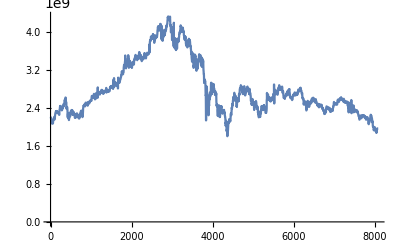

```mathematica
ListLinePlot[twapsWethUsdc90dFiltered8Week, PlotRange->All]
```

```mathematica
(* Estimate fits for each span of time *)
```

```mathematica
rsWethUsdc90dFiltered1Week = Differences[Log[twapsWethUsdc90dFiltered1Week]]
```

{-0.00120673,0.000176452,-0.0000603568,-0.000373722,-0.000389599,0.000559858,-0.00092094,-0.00154871,-0.000905547,-0.000584311,-0.00172231,-0.00371162,-0.00218903,-0.00259613,-0.00374997,-0.00385087,-0.00499694,-0.00681335,-0.00674886,-0.00538641,-0.00238816,0.0014468,0.00178939,0.000805576,-0.0000377299,-0.00155115,-0.00338662,-0.00382918,-0.00321668,-0.00270154,-0.00132964,0.000186854,0.00248069,0.00193942,0.00361139,0.00131712,0.00210643,0.00262488,0.00257794,0.00174097,0.00254967,0.00294714,0.00224079,0.00201131,0.00100575,-0.00125599,-0.00167678,-0.00119665,-0.00236811,-0.00157824,-0.00332412,-0.00354818,-0.00450461,-0.00398038,-0.00322619,-0.00304323,0.000142204,0.000979734,0.0021921,0.00450208,0.00447003,0.00571894,0.00373655,0.00548546,0.00235632,0.00100711,0.00263737,0.000611337,-0.000136787,3.23868×10^-6,0.000777499,0.00199232,0.00303221,0.00327366,0.0033268,0.00307257,0.00216783,0.000783838,-0.000080765,0.000712625,0.000341638,-0.00024731,-0.00129321,-0.000717748,-0.0014396,-0.000834414,0.0000370664,0.000883407,0.00188126,0.00330856,0.0033331,0.00375294,0.00315136,0.000968898,-0.000801161,-0.00274671,-0.00394275,-0.00478984,-0.00467682,-0.00443888,-0.00235901,-0.000880246,0.00120961,0.00528268,0.00433957,0.00635964,0.00568107,0.00541609,0.00487764,0.00308507,0.00410442,0.00120017,0.00197393,0.00275295,0.00157799,0.00366619,0.00206488,0.00133458,0.000382621,-0.0000699762,0.00016049,0.00183379,0.00206868,0.00300834,0.00278611,0.00253281,0.00150304,0.0000776621,-0.000766576,-0.000219429,0.00062098,0.000245869,0.00224434,0.00260876,0.00210895,0.000646611,0.00125299,-4.26556×10^-6,-0.00153047,-0.00196873,-0.000776981,-0.000962884,0.00028361,0.0000302359,0.000690131,0.0000496851,0.00153279,0.00162621,0.00174437,0.000266823,-0.0012285,-0.00483641,-0.00409798,-0.00398706,-0.00134311,0.000485584,0.00229321,0.00220958,0.000161885,-0.0000742672,0.000928476,0.000205861,0.00101243,0.000866467,0.000885114,-0.000199799,-0.00127449,-0.00280245,-0.0033278,-0.00277031,-0.000607151,-0.00189991,0.000708547,0.000977043,0.00122085,0.000341527,0.000403759,-0.000586693,-0.000678702,-0.000395253,0.000632638,0.000902484,0.00103304,0.00270694,0.00160654,-0.000847635,-0.00119222,-0.00175055,-0.00249942,-0.00194127,-0.00137353,-0.0013237,-0.000759113,-0.000822173,-0.000615807,0.00114548,0.00105966,0.000674579,0.00162314,0.00101654,0.000823438,0.00060543,-0.000267887,-0.000910003,-0.00234046,-0.00258329,-0.00313232,-0.00231122,-0.00201389,-0.0022762,-0.00161991,-0.00147791,-0.0000243955,0.00067665,0.0060331,0.00668285,0.00927214,0.00797051,0.00902686,0.00389741,0.00219452,0.00210222,0.000445539,0.00103525,0.00128522,0.000247569,0.0011596,0.00361498,0.00495561,0.00529279,0.00420697,0.00408244,0.000438949,-0.000374359,-0.000597394,0.00204706,0.00254348,0.00195034,0.0000247282,-0.000905713,-0.00238829,-0.00181462,-0.000955324,-0.00165848,-0.00166356,-0.000448398,-0.0000418368,-0.000962198,-0.000526023,-0.000771889,-0.00113149,-0.00087899,0.000785294,0.00210836,0.00254428,0.00193499,0.000597359,-0.000959418,-0.00173637,-0.00221478,-0.0032536,-0.00200872,-0.00166366,-0.00528351,0.00228401,-0.000396164,-0.00140414,-0.00116982,0.00374935,-0.00420261,-0.00273237,-0.00157084,-0.00223279,-0.00405097,-0.00261365,0.000508622,0.00103635,-0.000164515,-0.0000628882,-0.000951101,-0.000162466,0.000665113,0.00251147,0.00592911,0.00806295,0.00596692,0.00549004,0.00330576,-0.000737829,-0.00550944,-0.00680145,-0.00387939,-0.00231952,0.000446972,0.00514113,0.0043007,0.00136402,-0.00100532,-0.00136694,-0.00138374,-0.00102386,0.000420436,0.00251006,0.00290296,0.00302551,0.00287687,0.00101647,0.00130164,0.0009427,0.00163272,0.00355894,0.00254027,0.00534872,0.00328251,0.000504665,-0.000189969,-0.000860302,-0.00234141,-0.00133308,-0.000212404,-0.000577845,-0.000651895,-0.000569861,-0.00188448,-0.00219684,-0.00299699,-0.00218893,-0.00093305,0.00102137,0.00148281,0.00397436,0.00296892,0.00417452,0.00277819,0.0021355,0.00139401,0.00222117,0.00218928,0.00276008,0.00360778,0.00444973,0.00416209,0.00330268,0.00318243,0.0027957,0.00224798,0.00145072,0.00158945,0.000651551,-0.00122243,-0.00100825,-0.0001823,0.0000705225,-0.000749663,-0.000746842,0.000326147,-0.000404649,0.00054826,0.00273891,0.00300199,0.00219743,0.00106368,0.000615812,-0.000113195,0.000718815,0.0022022,0.00261939,0.0036032,0.00383303,-0.000961861,-0.00216249,-0.00328255,-0.00409711,-0.0126016,-0.00504819,-0.00349995,-0.000706687,0.00103729,0.00136636,-0.00120346,-0.00338883,-0.00431124,-0.00296884,-0.00108496,0.0000695733,0.00142483,-0.0023581,-0.00553602,-0.00727636,-0.0092007,-0.0118317,-0.0107324,-0.00400684,-0.00258077,-0.000348289,0.00414171,0.00622641,0.00211121,0.000154442,0.000745415,-0.000588753,-0.00172617,-0.000141715,0.00208687,0.00152084,0.0015393,-0.000833912,-0.00201515,-0.00103073,0.000283345,-0.00115785,-0.00157559,-0.00214027,-0.00500302,-0.00799012,-0.00601438,-0.00694454,-0.00459589,-0.00846632,-0.0138003,-0.0127245,-0.00823448,-0.00693386,3.57542×10^-6,-0.00603135,0.0156081,0.00445268,0.0027864,0.00281029,0.0101999,-0.0114221,-0.000911608,-0.00357121,-0.0062516,-0.00219527,-0.00662301,-0.00450093,-0.000491038,0.00115676,0.000382632,0.00306648,-0.00141802,-0.00508591,-0.0033121,-0.00198609,0.000196775,0.00318695,0.00105543,-0.00314687,-0.00493772,-0.0062809,-0.00669001,-0.00197024,0.002545,0.00397548,0.00664627,0.00506877,0.00290276,0.000112059,0.000552199,-0.000258701,0.00278543,0.00554231,0.00672165,0.00870246,0.0058659,0.00278655,0.00256674,0.00239826,0.00237098,0.00120443,0.00266766,-0.000104853,-0.00174875,-0.00361806,-0.00177669,-0.00377022,-0.00261829,-0.00314037,-0.00395221,-0.00546506,-0.00215465,-0.00114284,0.00177262,0.00463417,0.00691103,0.00487133,0.00370479,0.00227567,-0.000406678,0.000569698,0.00289343,0.00389197,0.00468766,0.00583437,0.00210819,0.00231993,0.000128694,-0.000935311,-0.00134891,-0.000956703,-0.00512835,-0.00246365,-0.000600981,-0.000159904,0.00141108,0.00515938,0.00353114,0.00427087,0.00242524,0.00106617,0.00053809,0.000319866,0.00174101,0.00169106,0.00115526,0.00099856,-0.00089797,-0.00263275,-0.00228707,-0.000550966,-0.00118163,-0.00124948,-0.000957185,-0.00252525,-0.00283688,-0.00256824,-0.00164856,0.000120219,0.00140416,0.00139857,0.00220359,0.00216545,0.00178297,0.0033324,0.00215588,-0.00109466,0.00139342,-0.00942686,-0.00789698,-0.00787459,-0.00469481,-0.00744448,0.00384828,0.000848758,0.000367058,-0.00213207,-0.00301034,-0.00183259,0.000645233,0.000492977,0.00390305,0.00656524,0.00370489,0.00413998,0.00228553,0.000542292,-0.00167351,-0.000141523,-0.000404621,0.000174401,0.000815721,0.00153486,-0.000492745,-0.000207424,-0.000332305,-0.0000290578,0.000860051,0.00107633,0.00105768,-0.000115579,-0.00192669,-0.00277235,-0.0024697,-0.00431359,-0.00412185,-0.00118579,-0.000975521,-0.000461467,0.000589419,0.00163457,0.00169184,0.0014601,0.00180705,-0.000527823,-0.00163603,-0.00307266,-0.00280879,-0.00282746,-0.00119031,-0.00259338,-0.00269458,-0.00441814,-0.00421308,-0.00487301,-0.00384606,-0.0024068,-0.00116728,-0.00062649,-0.00235755,-0.001129,0.00020115,-0.000197578,-0.000657545,0.00420281,0.00501052,0.00178519,0.00206233,0.00162655,-0.000448803,-0.00122814,-0.000879599,-0.00228374,-0.00145558,-0.00227247,-0.000861159,-0.000950716,-0.00165397,-0.000283907,0.00123609,0.00278327,0.00346455,0.00732741,0.00421292,0.0022428,0.00119173,-0.000244369,-0.000938577,-0.000866448,-0.00315846,-0.00195881,-0.000822664,0.000449665,0.00176114,0.00654132,0.00442676,0.00273136,0.00219691,0.00225034,-0.000494392,-0.000455288,0.0000653734,0.000162442,-0.000293995,-0.00113959,-0.000445806,0.000559219,0.00113625,0.00165103,0.0023337,0.00167441,0.00038733,-0.000264483,-0.00014555,-0.000721203,-0.0013545,-0.00131775,-0.00148765,-0.00368341,-0.00255773,-0.00183317,-0.00110648,-0.00184839,-0.00357169,-0.00268691,-0.00135763,-0.00118826,-0.00259678,-0.000441151,-0.000689152,-0.00106823,-0.00101267,0.00155722,0.00191746,0.0023195,0.00228884,0.00135436,0.000287349,0.000402753,0.000133519,0.000359978,0.000207549,-0.000834001,-0.00217155,-0.00214295,-0.00421486,-0.00481491,-0.00414322,-0.00272072,-0.00224655,-0.00133937,-0.000807712,0.0002067,0.000593348,0.000970919,0.00145467,0.00165921,0.000482959,0.000376061,0.000136985,-0.000109334,-0.000126934,-0.000581944,-0.000879138,-0.00206599,-0.0018632,-0.00180305,-0.000997964,0.000552587,0.000589507,0.00114622,0.00215245,0.00119253,0.0027759,0.00384843,0.00323833,0.00188691,0.000715281,-0.00139645,0.00138431,0.0028638,0.00487441,0.00650475,0.00572486,0.00190231,0.000508831,-0.00163774,-0.00105941,0.000355478,0.000561101,0.0017383,0.00239054,0.00275324,0.00379113,0.00269575,0.00209498,0.00234747,0.000789187,0.000888326,0.00106607,0.0000390036,-0.0000525149,-0.0000821205,-0.000556964,0.000461147,0.00167898,0.00102753,0.00253293,0.00325176,0.00215814,0.00165608,0.000163246,0.000269869,0.000040018,-0.00118776,-0.000608973,0.000444086,0.000266682,0.0000139491,0.00115176,-0.000157003,-0.0018536,-0.00156399,-0.00143625,-0.00181795,-0.00172224,-0.000951319,-0.0027338,-0.00290476,-0.00252172,-0.00194732,-0.0004145,-0.000291751,0.000606317,-0.000385714,-0.00267611,-0.0025355,-0.00115107,-0.00132192,-0.00200004,-0.00457616,-0.00559553,-0.00429184,-0.00661355,-0.00646869,-0.00155098,0.000668081,0.000853597,0.00374922,0.00604024,0.00552838,0.00478614,0.00206674,0.00275674,0.00438478,0.00272398,0.00193095,0.00311733,0.00756794,0.00913441,0.00897017,0.00804286,0.0077439,0.00482622,0.00199162,0.00162826,0.00249967,0.00292999,0.00318709,0.00334572,0.000962092,-0.000387674,-0.000873219,-0.000166592,-0.000589148,0.00165579,0.00136832,0.000670425,-0.0000450499,0.000227281,0.00097717,0.00165013,0.00142033,0.000842973,0.000234833,-0.000560104,-0.00218888,-0.00153094,-0.000487778,0.0000201364,0.000171513,0.00236449,0.00259948,0.00211419,0.00243991,0.00193531,-0.000109346,-0.00162508,-0.00240107,-0.00241968,-0.00186829,-0.00116043,-0.000866059,-0.00110812,-0.0011947,-0.00158624,-0.00124399,-0.000265758,-0.000294621,-0.00092884,-0.000592053,0.00221002,0.00327831,0.00304925,0.00529694,0.00459602,0.00108425,0.000509407,0.00060931,0.00127141,0.0015676,0.00223282,0.00302034,0.00244967,0.000842439,-0.000652185,-0.000480236,-0.000902864,-0.00203126,-0.00120842,-0.00174557,-0.00179562,-0.000365795,0.000516376,0.000600133,0.000788552,-0.0000507764,-0.00205586,-0.000868774,-0.000639892,-0.000710718,-0.0000478221,0.000538015,0.000799382,0.00141177,0.000242582,-0.000230628,-0.00222298,-0.0016392,-0.00211303,0.00115072,0.00293122,0.00471373,0.00239054,0.00279118,0.000304917,-0.000603432,-0.00208368,-0.00169736,-0.00124682,-0.0012971,-0.000776473,-0.00064134,-0.000571684,-0.000610072,-0.000415267,-0.000689104,-0.0010389,-0.00104936,-0.00114247,-0.00389013,-0.00287061,-0.00345415,-0.00146925,0.000809617,0.00315623,0.00449341,0.0077896,0.00491217,0.00285559,0.00159224,0.00154276,-0.000965606,-0.000133131,-0.0000589046,0.000575507,0.00130704,0.00118483,-0.000446293,-0.000308394,-0.00101341,-0.00121398,-0.00184522,-0.000121873,-0.0000669166,0.000202302,0.000011791,0.0000613097,0.000877181,0.00092317,0.000681095,0.00102483,0.000978949,0.000449505,-0.000546981,-0.00178726,-0.0019691,-0.00237213,-0.00218041,-0.00175071,-0.000352776,0.000179633,0.000135227,0.000288145,0.000817332,0.00144868,0.0020547,0.00232534,0.00244505,0.00120557,0.00133906,0.00287408,0.00157919,0.00204595,0.00179106,0.00192126,0.000724835,0.000382512,0.000375168,-0.000228686,-0.000503744,-0.000898399,-0.000763558,-0.000607949,-0.000116725,-0.000199824,0.0000961991,-0.000569861,-0.000306774,-0.000210067,0.000307569,0.000141434,0.000924759,0.000448156,-0.000084335,-0.000202221,-0.00025325,-0.000526525,-0.000136104,0.000788527,0.000945125,0.00114049,0.00157497,0.00167556,0.00135261,0.00159875,0.000749986,0.0000842274,-0.000902854,-0.00104242,-0.00116856,-0.000918878,-0.000989948,-0.000842766,-0.0010209,-0.00102635,0.000980125}

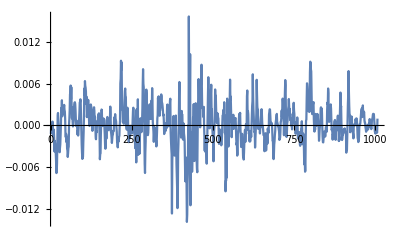

```mathematica
ListLinePlot[rsWethUsdc90dFiltered1Week, PlotRange->All]
```

```mathematica
edistWethUsdc90dFiltered1Week= EstimatedDistribution[rsWethUsdc90dFiltered1Week, StableDistribution[1, aWU90dF1W, bWU90dF1W, locWU90dF1W, scaleWE90dF1W]]
```

StableDistribution[1,1.69578,-0.00768849,0.000175309,0.0016727]

```mathematica
rsWethUsdc90dFiltered2Week = Differences[Log[twapsWethUsdc90dFiltered2Week]]
```

{-0.00120673,0.000176452,-0.0000603568,-0.000373722,-0.000389599,0.000559858,-0.00092094,-0.00154871,-0.000905547,-0.000584311,-0.00172231,-0.00371162,-0.00218903,-0.00259613,-0.00374997,-0.00385087,-0.00499694,-0.00681335,-0.00674886,-0.00538641,-0.00238816,0.0014468,0.00178939,0.000805576,-0.0000377299,-0.00155115,-0.00338662,-0.00382918,-0.00321668,-0.00270154,-0.00132964,0.000186854,0.00248069,0.00193942,0.00361139,0.00131712,0.00210643,0.00262488,0.00257794,0.00174097,0.00254967,0.00294714,0.00224079,0.00201131,0.00100575,-0.00125599,-0.00167678,-0.00119665,-0.00236811,-0.00157824,-0.00332412,-0.00354818,-0.00450461,-0.00398038,-0.00322619,-0.00304323,0.000142204,0.000979734,0.0021921,0.00450208,0.00447003,0.00571894,0.00373655,0.00548546,0.00235632,0.00100711,0.00263737,0.000611337,-0.000136787,3.23868×10^-6,0.000777499,0.00199232,0.00303221,0.00327366,0.0033268,0.00307257,0.00216783,0.000783838,-0.000080765,0.000712625,0.000341638,-0.00024731,-0.00129321,-0.000717748,-0.0014396,-0.000834414,0.0000370664,0.000883407,0.00188126,0.00330856,0.0033331,0.00375294,0.00315136,0.000968898,-0.000801161,-0.00274671,-0.00394275,-0.00478984,-0.00467682,-0.00443888,-0.00235901,-0.000880246,0.00120961,0.00528268,0.00433957,0.00635964,0.00568107,0.00541609,0.00487764,0.00308507,0.00410442,0.00120017,0.00197393,0.00275295,0.00157799,0.00366619,0.00206488,0.00133458,0.000382621,-0.0000699762,0.00016049,0.00183379,0.00206868,0.00300834,0.00278611,0.00253281,0.00150304,0.0000776621,-0.000766576,-0.000219429,0.00062098,0.000245869,0.00224434,0.00260876,0.00210895,0.000646611,0.00125299,-4.26556×10^-6,-0.00153047,-0.00196873,-0.000776981,-0.000962884,0.00028361,0.0000302359,0.000690131,0.0000496851,0.00153279,0.00162621,0.00174437,0.000266823,-0.0012285,-0.00483641,-0.00409798,-0.00398706,-0.00134311,0.000485584,0.00229321,0.00220958,0.000161885,-0.0000742672,0.000928476,0.000205861,0.00101243,0.000866467,0.000885114,-0.000199799,-0.00127449,-0.00280245,-0.0033278,-0.00277031,-0.000607151,-0.00189991,0.000708547,0.000977043,0.00122085,0.000341527,0.000403759,-0.000586693,-0.000678702,-0.000395253,0.000632638,0.000902484,0.00103304,0.00270694,0.00160654,-0.000847635,-0.00119222,-0.00175055,-0.00249942,-0.00194127,-0.00137353,-0.0013237,-0.000759113,-0.000822173,-0.000615807,0.00114548,0.00105966,0.000674579,0.00162314,0.00101654,0.000823438,0.00060543,-0.000267887,-0.000910003,-0.00234046,-0.00258329,-0.00313232,-0.00231122,-0.00201389,-0.0022762,-0.00161991,-0.00147791,-0.0000243955,0.00067665,0.0060331,0.00668285,0.00927214,0.00797051,0.00902686,0.00389741,0.00219452,0.00210222,0.000445539,0.00103525,0.00128522,0.000247569,0.0011596,0.00361498,0.00495561,0.00529279,0.00420697,0.00408244,0.000438949,-0.000374359,-0.000597394,0.00204706,0.00254348,0.00195034,0.0000247282,-0.000905713,-0.00238829,-0.00181462,-0.000955324,-0.00165848,-0.00166356,-0.000448398,-0.0000418368,-0.000962198,-0.000526023,-0.000771889,-0.00113149,-0.00087899,0.000785294,0.00210836,0.00254428,0.00193499,0.000597359,-0.000959418,-0.00173637,-0.00221478,-0.0032536,-0.00200872,-0.00166366,-0.00528351,0.00228401,-0.000396164,-0.00140414,-0.00116982,0.00374935,-0.00420261,-0.00273237,-0.00157084,-0.00223279,-0.00405097,-0.00261365,0.000508622,0.00103635,-0.000164515,-0.0000628882,-0.000951101,-0.000162466,0.000665113,0.00251147,0.00592911,0.00806295,0.00596692,0.00549004,0.00330576,-0.000737829,-0.00550944,-0.00680145,-0.00387939,-0.00231952,0.000446972,0.00514113,0.0043007,0.00136402,-0.00100532,-0.00136694,-0.00138374,-0.00102386,0.000420436,0.00251006,0.00290296,0.00302551,0.00287687,0.00101647,0.00130164,0.0009427,0.00163272,0.00355894,0.00254027,0.00534872,0.00328251,0.000504665,-0.000189969,-0.000860302,-0.00234141,-0.00133308,-0.000212404,-0.000577845,-0.000651895,-0.000569861,-0.00188448,-0.00219684,-0.00299699,-0.00218893,-0.00093305,0.00102137,0.00148281,0.00397436,0.00296892,0.00417452,0.00277819,0.0021355,0.00139401,0.00222117,0.00218928,0.00276008,0.00360778,0.00444973,0.00416209,0.00330268,0.00318243,0.0027957,0.00224798,0.00145072,0.00158945,0.000651551,-0.00122243,-0.00100825,-0.0001823,0.0000705225,-0.000749663,-0.000746842,0.000326147,-0.000404649,0.00054826,0.00273891,0.00300199,0.00219743,0.00106368,0.000615812,-0.000113195,0.000718815,0.0022022,0.00261939,0.0036032,0.00383303,-0.000961861,-0.00216249,-0.00328255,-0.00409711,-0.0126016,-0.00504819,-0.00349995,-0.000706687,0.00103729,0.00136636,-0.00120346,-0.00338883,-0.00431124,-0.00296884,-0.00108496,0.0000695733,0.00142483,-0.0023581,-0.00553602,-0.00727636,-0.0092007,-0.0118317,-0.0107324,-0.00400684,-0.00258077,-0.000348289,0.00414171,0.00622641,0.00211121,0.000154442,0.000745415,-0.000588753,-0.00172617,-0.000141715,0.00208687,0.00152084,0.0015393,-0.000833912,-0.00201515,-0.00103073,0.000283345,-0.00115785,-0.00157559,-0.00214027,-0.00500302,-0.00799012,-0.00601438,-0.00694454,-0.00459589,-0.00846632,-0.0138003,-0.0127245,-0.00823448,-0.00693386,3.57542×10^-6,-0.00603135,0.0156081,0.00445268,0.0027864,0.00281029,0.0101999,-0.0114221,-0.000911608,-0.00357121,-0.0062516,-0.00219527,-0.00662301,-0.00450093,-0.000491038,0.00115676,0.000382632,0.00306648,-0.00141802,-0.00508591,-0.0033121,-0.00198609,0.000196775,0.00318695,0.00105543,-0.00314687,-0.00493772,-0.0062809,-0.00669001,-0.00197024,0.002545,0.00397548,0.00664627,0.00506877,0.00290276,0.000112059,0.000552199,-0.000258701,0.00278543,0.00554231,0.00672165,0.00870246,0.0058659,0.00278655,0.00256674,0.00239826,0.00237098,0.00120443,0.00266766,-0.000104853,-0.00174875,-0.00361806,-0.00177669,-0.00377022,-0.00261829,-0.00314037,-0.00395221,-0.00546506,-0.00215465,-0.00114284,0.00177262,0.00463417,0.00691103,0.00487133,0.00370479,0.00227567,-0.000406678,0.000569698,0.00289343,0.00389197,0.00468766,0.00583437,0.00210819,0.00231993,0.000128694,-0.000935311,-0.00134891,-0.000956703,-0.00512835,-0.00246365,-0.000600981,-0.000159904,0.00141108,0.00515938,0.00353114,0.00427087,0.00242524,0.00106617,0.00053809,0.000319866,0.00174101,0.00169106,0.00115526,0.00099856,-0.00089797,-0.00263275,-0.00228707,-0.000550966,-0.00118163,-0.00124948,-0.000957185,-0.00252525,-0.00283688,-0.00256824,-0.00164856,0.000120219,0.00140416,0.00139857,0.00220359,0.00216545,0.00178297,0.0033324,0.00215588,-0.00109466,0.00139342,-0.00942686,-0.00789698,-0.00787459,-0.00469481,-0.00744448,0.00384828,0.000848758,0.000367058,-0.00213207,-0.00301034,-0.00183259,0.000645233,0.000492977,0.00390305,0.00656524,0.00370489,0.00413998,0.00228553,0.000542292,-0.00167351,-0.000141523,-0.000404621,0.000174401,0.000815721,0.00153486,-0.000492745,-0.000207424,-0.000332305,-0.0000290578,0.000860051,0.00107633,0.00105768,-0.000115579,-0.00192669,-0.00277235,-0.0024697,-0.00431359,-0.00412185,-0.00118579,-0.000975521,-0.000461467,0.000589419,0.00163457,0.00169184,0.0014601,0.00180705,-0.000527823,-0.00163603,-0.00307266,-0.00280879,-0.00282746,-0.00119031,-0.00259338,-0.00269458,-0.00441814,-0.00421308,-0.00487301,-0.00384606,-0.0024068,-0.00116728,-0.00062649,-0.00235755,-0.001129,0.00020115,-0.000197578,-0.000657545,0.00420281,0.00501052,0.00178519,0.00206233,0.00162655,-0.000448803,-0.00122814,-0.000879599,-0.00228374,-0.00145558,-0.00227247,-0.000861159,-0.000950716,-0.00165397,-0.000283907,0.00123609,0.00278327,0.00346455,0.00732741,0.00421292,0.0022428,0.00119173,-0.000244369,-0.000938577,-0.000866448,-0.00315846,-0.00195881,-0.000822664,0.000449665,0.00176114,0.00654132,0.00442676,0.00273136,0.00219691,0.00225034,-0.000494392,-0.000455288,0.0000653734,0.000162442,-0.000293995,-0.00113959,-0.000445806,0.000559219,0.00113625,0.00165103,0.0023337,0.00167441,0.00038733,-0.000264483,-0.00014555,-0.000721203,-0.0013545,-0.00131775,-0.00148765,-0.00368341,-0.00255773,-0.00183317,-0.00110648,-0.00184839,-0.00357169,-0.00268691,-0.00135763,-0.00118826,-0.00259678,-0.000441151,-0.000689152,-0.00106823,-0.00101267,0.00155722,0.00191746,0.0023195,0.00228884,0.00135436,0.000287349,0.000402753,0.000133519,0.000359978,0.000207549,-0.000834001,-0.00217155,-0.00214295,-0.00421486,-0.00481491,-0.00414322,-0.00272072,-0.00224655,-0.00133937,-0.000807712,0.0002067,0.000593348,0.000970919,0.00145467,0.00165921,0.000482959,0.000376061,0.000136985,-0.000109334,-0.000126934,-0.000581944,-0.000879138,-0.00206599,-0.0018632,-0.00180305,-0.000997964,0.000552587,0.000589507,0.00114622,0.00215245,0.00119253,0.0027759,0.00384843,0.00323833,0.00188691,0.000715281,-0.00139645,0.00138431,0.0028638,0.00487441,0.00650475,0.00572486,0.00190231,0.000508831,-0.00163774,-0.00105941,0.000355478,0.000561101,0.0017383,0.00239054,0.00275324,0.00379113,0.00269575,0.00209498,0.00234747,0.000789187,0.000888326,0.00106607,0.0000390036,-0.0000525149,-0.0000821205,-0.000556964,0.000461147,0.00167898,0.00102753,0.00253293,0.00325176,0.00215814,0.00165608,0.000163246,0.000269869,0.000040018,-0.00118776,-0.000608973,0.000444086,0.000266682,0.0000139491,0.00115176,-0.000157003,-0.0018536,-0.00156399,-0.00143625,-0.00181795,-0.00172224,-0.000951319,-0.0027338,-0.00290476,-0.00252172,-0.00194732,-0.0004145,-0.000291751,0.000606317,-0.000385714,-0.00267611,-0.0025355,-0.00115107,-0.00132192,-0.00200004,-0.00457616,-0.00559553,-0.00429184,-0.00661355,-0.00646869,-0.00155098,0.000668081,0.000853597,0.00374922,0.00604024,0.00552838,0.00478614,0.00206674,0.00275674,0.00438478,0.00272398,0.00193095,0.00311733,0.00756794,0.00913441,0.00897017,0.00804286,0.0077439,0.00482622,0.00199162,0.00162826,0.00249967,0.00292999,0.00318709,0.00334572,0.000962092,-0.000387674,-0.000873219,-0.000166592,-0.000589148,0.00165579,0.00136832,0.000670425,-0.0000450499,0.000227281,0.00097717,0.00165013,0.00142033,0.000842973,0.000234833,-0.000560104,-0.00218888,-0.00153094,-0.000487778,0.0000201364,0.000171513,0.00236449,0.00259948,0.00211419,0.00243991,0.00193531,-0.000109346,-0.00162508,-0.00240107,-0.00241968,-0.00186829,-0.00116043,-0.000866059,-0.00110812,-0.0011947,-0.00158624,-0.00124399,-0.000265758,-0.000294621,-0.00092884,-0.000592053,0.00221002,0.00327831,0.00304925,0.00529694,0.00459602,0.00108425,0.000509407,0.00060931,0.00127141,0.0015676,0.00223282,0.00302034,0.00244967,0.000842439,-0.000652185,-0.000480236,-0.000902864,-0.00203126,-0.00120842,-0.00174557,-0.00179562,-0.000365795,0.000516376,0.000600133,0.000788552,-0.0000507764,-0.00205586,-0.000868774,-0.000639892,-0.000710718,-0.0000478221,0.000538015,0.000799382,0.00141177,0.000242582,-0.000230628,-0.00222298,-0.0016392,-0.00211303,0.00115072,0.00293122,0.00471373,0.00239054,0.00279118,0.000304917,-0.000603432,-0.00208368,-0.00169736,-0.00124682,-0.0012971,-0.000776473,-0.00064134,-0.000571684,-0.000610072,-0.000415267,-0.000689104,-0.0010389,-0.00104936,-0.00114247,-0.00389013,-0.00287061,-0.00345415,-0.00146925,0.000809617,0.00315623,0.00449341,0.0077896,0.00491217,0.00285559,0.00159224,0.00154276,-0.000965606,-0.000133131,-0.0000589046,0.000575507,0.00130704,0.00118483,-0.000446293,-0.000308394,-0.00101341,-0.00121398,-0.00184522,-0.000121873,-0.0000669166,0.000202302,0.000011791,0.0000613097,0.000877181,0.00092317,0.000681095,0.00102483,0.000978949,0.000449505,-0.000546981,-0.00178726,-0.0019691,-0.00237213,-0.00218041,-0.00175071,-0.000352776,0.000179633,0.000135227,0.000288145,0.000817332,0.00144868,0.0020547,0.00232534,0.00244505,0.00120557,0.00133906,0.00287408,0.00157919,0.00204595,0.00179106,0.00192126,0.000724835,0.000382512,0.000375168,-0.000228686,-0.000503744,-0.000898399,-0.000763558,-0.000607949,-0.000116725,-0.000199824,0.0000961991,-0.000569861,-0.000306774,-0.000210067,0.000307569,0.000141434,0.000924759,0.000448156,-0.000084335,-0.000202221,-0.00025325,-0.000526525,-0.000136104,0.000788527,0.000945125,0.00114049,0.00157497,0.00167556,0.00135261,0.00159875,0.000749986,0.0000842274,-0.000902854,-0.00104242,-0.00116856,-0.000918878,-0.000989948,-0.000842766,-0.0010209,-0.00102635,0.000980125,0.00466948,0.00435123,0.00699025,0.00655278,0.00483603,0.00138255,0.00181332,0.00206437,0.00261004,0.00139139,0.0026052,0.000192994,-0.000594479,-0.00191702,-0.000874915,-0.00177684,-0.00119709,-0.00118025,0.0000498224,-0.0000695999,-0.000173381,-0.000463836,0.000109768,0.000148284,-0.000310118,0.000274326,0.000552073,-0.00118885,-0.00203713,-0.00186567,-0.000657554,-0.000552606,0.000677591,0.00176288,0.00167314,0.000343884,0.000628297,0.000467979,-0.000348427,0.0006145,0.00054536,-0.000128062,-0.000416618,-0.000521026,-0.0015129,-0.00191137,-0.000968557,0.0000143828,0.00106242,0.00156105,0.00297838,0.00404862,0.00454336,0.00323331,0.00278779,0.00188643,0.00074969,0.000215854,0.000703627,0.00120311,0.0015477,0.00117297,0.00119751,-0.0000595017,-0.00130719,-0.00275445,-0.00369014,-0.00390995,-0.00416706,-0.00331629,-0.00267624,-0.00124081,-0.000435451,0.00023022,0.000462324,0.000644081,-0.000343244,-0.000732279,-0.000314967,-0.000838453,-0.0024047,-0.000602897,-0.00200062,-0.00429456,-0.00314678,-0.00368357,-0.000863389,-0.00298032,0.000781605,0.00146051,0.00267362,0.00156457,0.00253169,0.00152362,0.00112573,0.000719234,0.000428393,0.000405166,-0.000222705,-0.0015047,-0.00186106,-0.002133,-0.00157837,0.0000362676,0.000672393,0.00185016,0.00217979,0.00179423,0.0016508,0.00283524,0.00313298,0.00340067,0.00455065,0.00579742,0.00377328,0.00360246,0.00312079,0.00222869,0.00140936,0.000989776,0.00169525,-0.00242705,-0.00209561,-0.0018528,-0.00209557,-0.000946723,0.00186983,0.00171426,0.00196074,0.00149224,0.00033871,-0.00115616,-0.00189843,-0.00357131,-0.00211127,-0.00228,-0.000137593,0.000618353,0.00150091,0.00170323,0.00267142,0.00171991,0.00190605,0.00151379,0.00109552,0.000747929,-8.32535×10^-6,-0.0000696488,0.00123753,0.00114301,0.000810575,-0.0414512,0.0419846,-0.000682734,-0.0011462,-0.0000871902,0.041082,-0.0388866,-0.0086889,0.00695421,-0.000777239,-0.00195428,-0.00185956,0.00843883,-0.0090184,-0.0000178437,0.0012989,0.00316076,0.00380601,0.00280303,0.000709552,-0.000329469,-0.00221543,-0.00344843,-0.00155582,-0.000329168,-0.0000441934,0.000735073,0.00259507,0.00167799,0.00139987,0.00114346,0.00037167,-0.000835275,-0.00126008,-0.00214914,-0.00193602,-0.00151427,-0.00155432,-0.000963495,0.000344132,0.000623351,0.000445749,0.000462623,0.0000709405,-0.000302673,-0.000857178,-0.000336417,-0.000315789,-0.000821418,-0.00233291,-0.00191269,-0.0022671,-0.00199191,-0.000830382,-0.000560195,-0.0000881161,0.000826126,0.00100014,0.000773918,0.0017694,0.00187312,0.0014366,0.00149527,0.00126627,0.00209366,0.00110499,0.00131611,0.000622154,0.00024545,0.000265324,0.000329664,-0.000106138,-0.000108165,-0.00056995,-0.00112594,-0.000854892,-0.00109436,-0.00102154,0.00100342,0.00273074,0.00301677,0.0037619,0.00375775,0.00245633,0.000342655,0.000150083,-0.000116608,-0.000196338,0.000114894,0.000638325,0.000272947,0.0000955498,0.000132804,-0.000321559,-0.000631006,0.000643513,0.0013194,0.00149388,0.00202969,0.0021509,0.000318524,-0.00045603,-0.00101728,-0.00158425,-0.00245614,-0.00157256,-0.00106742,-0.000512263,0.000120067,0.000483341,0.000529602,0.000982815,0.00175016,0.00120714,0.00128144,0.00122909,-0.000382203,-0.00189347,-0.002069,-0.00248612,-0.00286884,-0.00371627,-0.00223168,-0.00119364,-0.00124053,0.00021558,-0.000951067,-0.00183928,-0.00191845,-0.00145192,-0.00188646,0.00106149,0.00129213,0.00103251,0.000932346,0.000880728,-0.0000126498,-0.0016209,-0.00262868,-0.00101439,-0.000917749,-0.00153729,0.0000288463,0.00102805,0.0000462368,-0.000223226,0.00117025,0.00220649,0.0026161,0.0029575,0.00270385,0.00283155,0.0017771,0.00154787,0.000945675,0.000489633,0.000191487,-0.0000167517,-0.00015439,-0.000620863,-0.00180333,-0.000406361,-0.00101402,-0.00116203,-0.00121671,-0.000429419,-0.00150654,-0.000298645,0.000396086,0.00096187,0.000640243,0.000714087,-0.000611885,-0.000655001,-0.000031475,-0.000359274,-0.000301282,0.000208999,0.00048424,-0.000402084,0.000406336,0.000705886,0.00111772,0.00102443,0.00121048,0.0012271,0.000721953,0.000623852,0.000554546,0.000440623,0.000299463,0.000211864,0.000377373,0.000588372,0.0011471,0.00120216,0.00130684,0.00136994,0.00061367,-0.0000851429,-0.0000897249,-0.000529571,-0.000431752,-0.000831333,-0.000470113,-0.000540893,-0.000233389,0.000474922,0.00121517,0.0012423,0.00687042,-0.00439132,-0.00022816,-0.000427838,0.0145414,-0.0214728,0.00490606,-0.000106052,-0.00109714,-0.0178032,0.0139376,-0.001578,-0.00204077,-0.00145424,-0.000911688,-0.000986064,-0.000957783,-0.00063972,0.000279193,0.000616705,0.000661391,-0.000181405,-0.000182426,-0.000452632,-0.000701488,-0.00100204,0.000828089,0.000936799,0.00119491,0.00142162,0.000730048,-0.0010337,-0.00064549,-0.000901503,-0.000834874,-0.0000124756,-0.000112099,0.0000744141,0.000335802,0.000209805,0.000403169,0.00145046,0.00136271,0.00110441,0.000845306,0.000787364,-0.0000138236,0.000380087,-0.0000181431,9.66408×10^-6,0.000179784,-0.0000714102,-0.000309686,0.000421643,0.00117555,0.00122649,0.00100583,0.000777633,0.000476592,-0.0000828325,-0.000651464,-0.000751128,-0.000666225,-0.000875066,-0.000950376,-0.000825752,-0.00130323,-0.000730362,-0.000554217,-0.000474488,-0.000175335,0.000199862,-0.00040209,-0.000365556,-0.00054007,-0.0000890267,-0.000144091,0.000480641,0.000898759,0.00121699,0.0013267,0.00146877,0.000785515,0.000415181,0.000110056,-0.0000248417,-0.000334675,-0.000252165,-0.000479,-0.0000305659,0.000414973,0.00384283,0.00464208,0.00459038,0.00368655,0.00497468,0.000773252,1.38813×10^-6,-0.000248345,0.000728654,0.000632891,0.000806726,0.00112336,0.000978499,0.000167927,-0.0000516025,-0.000132285,-0.000172418,-0.0000546051,0.00107165,0.00164232,0.00173899,0.00117991,0.00128991,-0.000548989,-0.000770046,-0.00104571,-0.000414962,0.00026135,0.000389526,0.000108301,0.0000929041,-0.000114462,-0.000323705,-0.000126862,0.000330517,0.000496064,0.000213113,-0.000167446,-0.00139237,-0.00272959,-0.00232198,-0.00172782,-0.000684152,0.000231279,0.000995399,0.00050165,-0.000188684,-0.000769504,-0.0000244679,0.00099389,0.00124882,0.00156672,0.00141812,0.00113295,0.000454937,0.000420587,0.00130814,0.00155827,0.00131251,0.00135534,0.000837613,0.000137285,-0.000387778,-0.000451854,-0.000511923,-0.000313462,-0.00010025,-0.0000708208,-0.000263446,-0.000140434,-0.000482702,-0.000815066,-0.00112947,-0.000797436,-0.00134519,-0.000575632,0.000204589,0.00166638,0.0016478,0.00242032,0.00200975,-0.024293,0.0287025,0.00241599,0.00262571,0.00247084,0.0287808,-0.024599,0.00101865,0.00101533,0.000728176,0.000305472,0.000195423,0.000356933,0.000212255,-2.8602×10^-7,-0.000239674,-0.00103511,-0.00132637,-0.000243642,-0.000486028,0.000372106,0.00153891,0.0017067,0.00118684,0.0325148,-0.0323952,-0.00123801,-0.00107113,-0.000947338,-0.0272633,0.0274025,0.000942134,0.000724385,0.000939389,0.000352002,0.000550232,0.000914905,0.000628839,0.000935858,-0.00011343,-0.000281164,-0.000675134,-0.000591396,-0.000761658,-0.000398219,-0.000572141,-0.000255126,-0.0000255528,0.0000943235,0.00038541,0.000760633,0.00123961,0.000831282,0.000754185,0.000779138,0.000484623,0.0000428802,-0.000424447,-0.00208702,-0.00246332,-0.0039297,-0.00428938,-0.000577303,0.000242626,0.0000245399,0.000825934,0.00105264,-0.0000251619,-0.000716084,0.000179684,0.000199738,0.000297906,0.000168538,0.000115773,-0.000192196,-0.000645087,-0.00193845,-0.00193054,-0.00152017,-0.00167191,-0.00107768,-0.00121486,-0.00119745,-0.00173691,-0.00161948,-0.000748798,0.000209102,0.000428268,0.000734845,0.000650775,0.00106822,0.00124182,0.00227413,0.00236237,0.00269409,0.00165144,0.00127944,0.000140168,-0.000212721,-0.000154803,-0.0000187387,0.00024798,0.000754791,0.00119451,0.00112729,0.000954665,0.000378853,-0.000311067,-0.000222788,-0.000307194,0.0000524551,-0.00049898,-0.000822251,-0.000462705,-0.000779924,-0.000648556,0.0000669315,0.000405771,0.000312875,0.000132004,-0.0000905182,-0.0359786,0.0363046,0.000719188,0.000887844,0.00099192,0.0392383,-0.0373389,0.000206924,0.000342924,0.000147036,-0.0000812063,-0.0000587938,-0.000010622,0.0000676669,0.000470984,0.000573227,0.000683607,0.000486529,0.00116536,0.00137443,0.00126916,0.00221239,0.00210869,0.00136684,0.00111328,0.000556192,4.68688×10^-6,-0.000322991,-0.000525033,-0.000536487,-0.000511655,-0.000431705,0.000109535,0.000572768,0.000679499,0.000717861,0.0000733799,-0.0012067,-0.00178257,-0.00263177,-0.00309087,-0.00156029,-0.000561773,0.000348814,0.000448087,0.000741062,0.00179748,0.00209749,0.00311744,0.00242346,0.00295951,0.00106534,0.000726196,0.000531729,0.000642593,0.00207244,0.00198173,0.00145474,0.00181094,0.00119526,-0.0000490975,0.000415406,0.000611772,0.0014115,0.00154647,0.00167922,0.00156765,0.00175257,0.00165708,0.00100607,0.000475822,0.000133392,-0.000329116,-0.000433984,0.000604679,0.000488353,0.00172646,0.00300421,0.00327459,0.00199304,0.00110795,0.000996769,0.000117901,-0.000265054,-0.00057575,-0.000449893,0.000990467,0.0032076,0.00328159,0.00294208,0.00378181,0.00268727,0.00198293,0.00258181,0.00321178,0.00243213,0.00144033,-0.00101848,-0.00100298,-0.00112721,-0.000910306,0.000869275,-0.000377356,-0.00103542,-0.00152943,-0.001569,-0.00207574,-0.000185879,0.000708944,0.00165033,0.00164907,0.00174654,0.000590943,0.0000731581,-0.000917137,-0.00171684,-0.0026487,-0.00158419,-0.000924789,-0.00157356,-0.000800716,-0.000225496,-0.00233173,-0.00216651,-0.00138314,0.000223727,0.000821374,0.00270273,0.00422558,0.0033642,0.00176459,0.0024482,0.00168429,-0.0000629361,0.0000132796,0.00049209,-0.000300669,-0.000369268,0.00319694,0.00566947,0.00476461,0.00604239,0.00532524,0.00430516,0.0013428,0.00152603,0.00288647,0.00176983,0.00150136,0.00240793,0.00248646,0.00171193,-0.0000785452,-0.00165977,-0.000715552,-0.00111037,-0.00223867,-0.00109765,0.000818495,-0.00133836,-0.00203,-0.00011995,-0.0000860915,-0.000128324,0.0000563381,0.00117238,-0.000158133,0.00174783,0.00287387,0.00584965,0.00576358,0.00558716,0.00394461,0.00241308,0.0021106,0.00192353,0.00317306,0.00338297,0.00283384,0.0248727,-0.0295747,-0.00383283,-0.00312703,-0.00851689,-0.0327107,0.0239553,-0.00499594,-0.00491803,0.000593634,0.000786451,-0.00052929,-0.00289306,-0.0028111,-0.00220873,-0.00387005,-0.00423728,-0.000974656,-0.00045358,-0.00038493,0.00121984,0.000662481,0.000182991,0.00262872,0.00301494,0.00350616,0.00492893,0.00553839,0.00516567,0.00351876,0.00380111,0.00157244,0.00209146,0.00120385,0.000637409,0.000924354,0.00113682,-0.00025714,-0.00181377,-0.000730396,-0.000974799,-0.0012416,-0.00135503,-0.00119148,-0.00260131,-0.0040644,-0.00282087,-0.00174289,-0.00176069,-0.0014499,0.00222433,0.00218297,0.00380129,0.00368075,0.00269203,0.000260497,0.00085787,0.00160457,0.00182732,0.00401232,0.00475679,0.0026052,0.00121174,0.00205306,0.00300466,0.00256725,0.00305798,0.00237677,-0.0000541018,-0.00173103,0.000212214,-0.000311547,0.0023477,0.00313266,0.0144512,-0.00821527,-0.000233259,0.00056875,-0.0024141,-0.0136794,0.000907223,-0.00482629,-0.00769023,-0.00747064,-0.0072335,-0.00919936,-0.00783773,-0.00282945,-0.000552179,-0.0033097,-0.00492109,0.00136816,0.00209213,0.000817307,0.00210796,0.00522972,0.00402665,0.00189449,0.00252173,0.00251411,0.00316717,0.00382487,0.00245615,0.00212261,0.0024164,0.00348178,-0.0012568,0.00252062,0.00374274,-0.000014624,-0.0039969,0.00190518,-0.00181569,-0.00222069,0.000102459,-0.000351699,-0.00275528,-0.00307612,-0.0030861,-0.00445619,-0.00588402,-0.00278822,-0.00537252,-0.00111003,0.00106573,0.00149643,0.00119183,-0.00123869,-0.00321451,-0.00172741,-0.000772273,0.000197519,0.00399308,0.00389842,0.00285734,0.00352615,0.00349761,0.00249881,0.00279715,0.00276691,-0.000309147,-0.0000601254,-0.00173293,-0.00264434,-0.00202092,-0.00361974,-0.00439218,-0.00228394,-0.00179277,-0.00031246,-0.00038357,0.000503898,0.000934868,-0.000200978,-0.00243319,-0.00339921,-0.0025272,-0.00178304,0.0001005,0.000836132,0.000904455,0.0000406236,-0.00189845,-0.00266516,-0.00164924,-0.000771383,0.000356698,0.00163991,0.00280642,0.0033015,0.00506714,0.00617555,0.00352987,0.00374607,0.00350605}

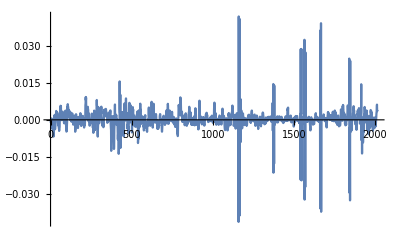

```mathematica
ListLinePlot[rsWethUsdc90dFiltered2Week, PlotRange->All]
```

```mathematica
edistWethUsdc90dFiltered2Week= EstimatedDistribution[rsWethUsdc90dFiltered2Week, StableDistribution[1, aWU90dF2W, bWU90dF2W, locWU90dF2W, scaleWE90dF2W]]
```

StableDistribution[1,1.5094,0.0433026,0.00027506,0.00136471]

```mathematica
rsWethUsdc90dFiltered4Week = Differences[Log[twapsWethUsdc90dFiltered4Week]]
```

{-0.00120673,0.000176452,-0.0000603568,-0.000373722,-0.000389599,0.000559858,-0.00092094,-0.00154871,-0.000905547,-0.000584311,-0.00172231,-0.00371162,-0.00218903,-0.00259613,-0.00374997,-0.00385087,-0.00499694,-0.00681335,-0.00674886,-0.00538641,-0.00238816,0.0014468,0.00178939,0.000805576,-0.0000377299,-0.00155115,-0.00338662,-0.00382918,-0.00321668,-0.00270154,-0.00132964,0.000186854,0.00248069,0.00193942,0.00361139,0.00131712,0.00210643,0.00262488,0.00257794,0.00174097,0.00254967,0.00294714,0.00224079,0.00201131,0.00100575,-0.00125599,-0.00167678,-0.00119665,-0.00236811,-0.00157824,-0.00332412,-0.00354818,-0.00450461,-0.00398038,-0.00322619,-0.00304323,0.000142204,0.000979734,0.0021921,0.00450208,0.00447003,0.00571894,0.00373655,0.00548546,0.00235632,0.00100711,0.00263737,0.000611337,-0.000136787,3.23868×10^-6,0.000777499,0.00199232,0.00303221,0.00327366,0.0033268,0.00307257,0.00216783,0.000783838,-0.000080765,0.000712625,0.000341638,-0.00024731,-0.00129321,-0.000717748,-0.0014396,-0.000834414,0.0000370664,0.000883407,0.00188126,0.00330856,0.0033331,0.00375294,0.00315136,0.000968898,-0.000801161,-0.00274671,-0.00394275,-0.00478984,-0.00467682,-0.00443888,-0.00235901,-0.000880246,0.00120961,0.00528268,0.00433957,0.00635964,0.00568107,0.00541609,0.00487764,0.00308507,0.00410442,0.00120017,0.00197393,0.00275295,0.00157799,0.00366619,0.00206488,0.00133458,0.000382621,-0.0000699762,0.00016049,0.00183379,0.00206868,0.00300834,0.00278611,0.00253281,0.00150304,0.0000776621,-0.000766576,-0.000219429,0.00062098,0.000245869,0.00224434,0.00260876,0.00210895,0.000646611,0.00125299,-4.26556×10^-6,-0.00153047,-0.00196873,-0.000776981,-0.000962884,0.00028361,0.0000302359,0.000690131,0.0000496851,0.00153279,0.00162621,0.00174437,0.000266823,-0.0012285,-0.00483641,-0.00409798,-0.00398706,-0.00134311,0.000485584,0.00229321,0.00220958,0.000161885,-0.0000742672,0.000928476,0.000205861,0.00101243,0.000866467,0.000885114,-0.000199799,-0.00127449,-0.00280245,-0.0033278,-0.00277031,-0.000607151,-0.00189991,0.000708547,0.000977043,0.00122085,0.000341527,0.000403759,-0.000586693,-0.000678702,-0.000395253,0.000632638,0.000902484,0.00103304,0.00270694,0.00160654,-0.000847635,-0.00119222,-0.00175055,-0.00249942,-0.00194127,-0.00137353,-0.0013237,-0.000759113,-0.000822173,-0.000615807,0.00114548,0.00105966,0.000674579,0.00162314,0.00101654,0.000823438,0.00060543,-0.000267887,-0.000910003,-0.00234046,-0.00258329,-0.00313232,-0.00231122,-0.00201389,-0.0022762,-0.00161991,-0.00147791,-0.0000243955,0.00067665,0.0060331,0.00668285,0.00927214,0.00797051,0.00902686,0.00389741,0.00219452,0.00210222,0.000445539,0.00103525,0.00128522,0.000247569,0.0011596,0.00361498,0.00495561,0.00529279,0.00420697,0.00408244,0.000438949,-0.000374359,-0.000597394,0.00204706,0.00254348,0.00195034,0.0000247282,-0.000905713,-0.00238829,-0.00181462,-0.000955324,-0.00165848,-0.00166356,-0.000448398,-0.0000418368,-0.000962198,-0.000526023,-0.000771889,-0.00113149,-0.00087899,0.000785294,0.00210836,0.00254428,0.00193499,0.000597359,-0.000959418,-0.00173637,-0.00221478,-0.0032536,-0.00200872,-0.00166366,-0.00528351,0.00228401,-0.000396164,-0.00140414,-0.00116982,0.00374935,-0.00420261,-0.00273237,-0.00157084,-0.00223279,-0.00405097,-0.00261365,0.000508622,0.00103635,-0.000164515,-0.0000628882,-0.000951101,-0.000162466,0.000665113,0.00251147,0.00592911,0.00806295,0.00596692,0.00549004,0.00330576,-0.000737829,-0.00550944,-0.00680145,-0.00387939,-0.00231952,0.000446972,0.00514113,0.0043007,0.00136402,-0.00100532,-0.00136694,-0.00138374,-0.00102386,0.000420436,0.00251006,0.00290296,0.00302551,0.00287687,0.00101647,0.00130164,0.0009427,0.00163272,0.00355894,0.00254027,0.00534872,0.00328251,0.000504665,-0.000189969,-0.000860302,-0.00234141,-0.00133308,-0.000212404,-0.000577845,-0.000651895,-0.000569861,-0.00188448,-0.00219684,-0.00299699,-0.00218893,-0.00093305,0.00102137,0.00148281,0.00397436,0.00296892,0.00417452,0.00277819,0.0021355,0.00139401,0.00222117,0.00218928,0.00276008,0.00360778,0.00444973,0.00416209,0.00330268,0.00318243,0.0027957,0.00224798,0.00145072,0.00158945,0.000651551,-0.00122243,-0.00100825,-0.0001823,0.0000705225,-0.000749663,-0.000746842,0.000326147,-0.000404649,0.00054826,0.00273891,0.00300199,0.00219743,0.00106368,0.000615812,-0.000113195,0.000718815,0.0022022,0.00261939,0.0036032,0.00383303,-0.000961861,-0.00216249,-0.00328255,-0.00409711,-0.0126016,-0.00504819,-0.00349995,-0.000706687,0.00103729,0.00136636,-0.00120346,-0.00338883,-0.00431124,-0.00296884,-0.00108496,0.0000695733,0.00142483,-0.0023581,-0.00553602,-0.00727636,-0.0092007,-0.0118317,-0.0107324,-0.00400684,-0.00258077,-0.000348289,0.00414171,0.00622641,0.00211121,0.000154442,0.000745415,-0.000588753,-0.00172617,-0.000141715,0.00208687,0.00152084,0.0015393,-0.000833912,-0.00201515,-0.00103073,0.000283345,-0.00115785,-0.00157559,-0.00214027,-0.00500302,-0.00799012,-0.00601438,-0.00694454,-0.00459589,-0.00846632,-0.0138003,-0.0127245,-0.00823448,-0.00693386,3.57542×10^-6,-0.00603135,0.0156081,0.00445268,0.0027864,0.00281029,0.0101999,-0.0114221,-0.000911608,-0.00357121,-0.0062516,-0.00219527,-0.00662301,-0.00450093,-0.000491038,0.00115676,0.000382632,0.00306648,-0.00141802,-0.00508591,-0.0033121,-0.00198609,0.000196775,0.00318695,0.00105543,-0.00314687,-0.00493772,-0.0062809,-0.00669001,-0.00197024,0.002545,0.00397548,0.00664627,0.00506877,0.00290276,0.000112059,0.000552199,-0.000258701,0.00278543,0.00554231,0.00672165,0.00870246,0.0058659,0.00278655,0.00256674,0.00239826,0.00237098,0.00120443,0.00266766,-0.000104853,-0.00174875,-0.00361806,-0.00177669,-0.00377022,-0.00261829,-0.00314037,-0.00395221,-0.00546506,-0.00215465,-0.00114284,0.00177262,0.00463417,0.00691103,0.00487133,0.00370479,0.00227567,-0.000406678,0.000569698,0.00289343,0.00389197,0.00468766,0.00583437,0.00210819,0.00231993,0.000128694,-0.000935311,-0.00134891,-0.000956703,-0.00512835,-0.00246365,-0.000600981,-0.000159904,0.00141108,0.00515938,0.00353114,0.00427087,0.00242524,0.00106617,0.00053809,0.000319866,0.00174101,0.00169106,0.00115526,0.00099856,-0.00089797,-0.00263275,-0.00228707,-0.000550966,-0.00118163,-0.00124948,-0.000957185,-0.00252525,-0.00283688,-0.00256824,-0.00164856,0.000120219,0.00140416,0.00139857,0.00220359,0.00216545,0.00178297,0.0033324,0.00215588,-0.00109466,0.00139342,-0.00942686,-0.00789698,-0.00787459,-0.00469481,-0.00744448,0.00384828,0.000848758,0.000367058,-0.00213207,-0.00301034,-0.00183259,0.000645233,0.000492977,0.00390305,0.00656524,0.00370489,0.00413998,0.00228553,0.000542292,-0.00167351,-0.000141523,-0.000404621,0.000174401,0.000815721,0.00153486,-0.000492745,-0.000207424,-0.000332305,-0.0000290578,0.000860051,0.00107633,0.00105768,-0.000115579,-0.00192669,-0.00277235,-0.0024697,-0.00431359,-0.00412185,-0.00118579,-0.000975521,-0.000461467,0.000589419,0.00163457,0.00169184,0.0014601,0.00180705,-0.000527823,-0.00163603,-0.00307266,-0.00280879,-0.00282746,-0.00119031,-0.00259338,-0.00269458,-0.00441814,-0.00421308,-0.00487301,-0.00384606,-0.0024068,-0.00116728,-0.00062649,-0.00235755,-0.001129,0.00020115,-0.000197578,-0.000657545,0.00420281,0.00501052,0.00178519,0.00206233,0.00162655,-0.000448803,-0.00122814,-0.000879599,-0.00228374,-0.00145558,-0.00227247,-0.000861159,-0.000950716,-0.00165397,-0.000283907,0.00123609,0.00278327,0.00346455,0.00732741,0.00421292,0.0022428,0.00119173,-0.000244369,-0.000938577,-0.000866448,-0.00315846,-0.00195881,-0.000822664,0.000449665,0.00176114,0.00654132,0.00442676,0.00273136,0.00219691,0.00225034,-0.000494392,-0.000455288,0.0000653734,0.000162442,-0.000293995,-0.00113959,-0.000445806,0.000559219,0.00113625,0.00165103,0.0023337,0.00167441,0.00038733,-0.000264483,-0.00014555,-0.000721203,-0.0013545,-0.00131775,-0.00148765,-0.00368341,-0.00255773,-0.00183317,-0.00110648,-0.00184839,-0.00357169,-0.00268691,-0.00135763,-0.00118826,-0.00259678,-0.000441151,-0.000689152,-0.00106823,-0.00101267,0.00155722,0.00191746,0.0023195,0.00228884,0.00135436,0.000287349,0.000402753,0.000133519,0.000359978,0.000207549,-0.000834001,-0.00217155,-0.00214295,-0.00421486,-0.00481491,-0.00414322,-0.00272072,-0.00224655,-0.00133937,-0.000807712,0.0002067,0.000593348,0.000970919,0.00145467,0.00165921,0.000482959,0.000376061,0.000136985,-0.000109334,-0.000126934,-0.000581944,-0.000879138,-0.00206599,-0.0018632,-0.00180305,-0.000997964,0.000552587,0.000589507,0.00114622,0.00215245,0.00119253,0.0027759,0.00384843,0.00323833,0.00188691,0.000715281,-0.00139645,0.00138431,0.0028638,0.00487441,0.00650475,0.00572486,0.00190231,0.000508831,-0.00163774,-0.00105941,0.000355478,0.000561101,0.0017383,0.00239054,0.00275324,0.00379113,0.00269575,0.00209498,0.00234747,0.000789187,0.000888326,0.00106607,0.0000390036,-0.0000525149,-0.0000821205,-0.000556964,0.000461147,0.00167898,0.00102753,0.00253293,0.00325176,0.00215814,0.00165608,0.000163246,0.000269869,0.000040018,-0.00118776,-0.000608973,0.000444086,0.000266682,0.0000139491,0.00115176,-0.000157003,-0.0018536,-0.00156399,-0.00143625,-0.00181795,-0.00172224,-0.000951319,-0.0027338,-0.00290476,-0.00252172,-0.00194732,-0.0004145,-0.000291751,0.000606317,-0.000385714,-0.00267611,-0.0025355,-0.00115107,-0.00132192,-0.00200004,-0.00457616,-0.00559553,-0.00429184,-0.00661355,-0.00646869,-0.00155098,0.000668081,0.000853597,0.00374922,0.00604024,0.00552838,0.00478614,0.00206674,0.00275674,0.00438478,0.00272398,0.00193095,0.00311733,0.00756794,0.00913441,0.00897017,0.00804286,0.0077439,0.00482622,0.00199162,0.00162826,0.00249967,0.00292999,0.00318709,0.00334572,0.000962092,-0.000387674,-0.000873219,-0.000166592,-0.000589148,0.00165579,0.00136832,0.000670425,-0.0000450499,0.000227281,0.00097717,0.00165013,0.00142033,0.000842973,0.000234833,-0.000560104,-0.00218888,-0.00153094,-0.000487778,0.0000201364,0.000171513,0.00236449,0.00259948,0.00211419,0.00243991,0.00193531,-0.000109346,-0.00162508,-0.00240107,-0.00241968,-0.00186829,-0.00116043,-0.000866059,-0.00110812,-0.0011947,-0.00158624,-0.00124399,-0.000265758,-0.000294621,-0.00092884,-0.000592053,0.00221002,0.00327831,0.00304925,0.00529694,0.00459602,0.00108425,0.000509407,0.00060931,0.00127141,0.0015676,0.00223282,0.00302034,0.00244967,0.000842439,-0.000652185,-0.000480236,-0.000902864,-0.00203126,-0.00120842,-0.00174557,-0.00179562,-0.000365795,0.000516376,0.000600133,0.000788552,-0.0000507764,-0.00205586,-0.000868774,-0.000639892,-0.000710718,-0.0000478221,0.000538015,0.000799382,0.00141177,0.000242582,-0.000230628,-0.00222298,-0.0016392,-0.00211303,0.00115072,0.00293122,0.00471373,0.00239054,0.00279118,0.000304917,-0.000603432,-0.00208368,-0.00169736,-0.00124682,-0.0012971,-0.000776473,-0.00064134,-0.000571684,-0.000610072,-0.000415267,-0.000689104,-0.0010389,-0.00104936,-0.00114247,-0.00389013,-0.00287061,-0.00345415,-0.00146925,0.000809617,0.00315623,0.00449341,0.0077896,0.00491217,0.00285559,0.00159224,0.00154276,-0.000965606,-0.000133131,-0.0000589046,0.000575507,0.00130704,0.00118483,-0.000446293,-0.000308394,-0.00101341,-0.00121398,-0.00184522,-0.000121873,-0.0000669166,0.000202302,0.000011791,0.0000613097,0.000877181,0.00092317,0.000681095,0.00102483,0.000978949,0.000449505,-0.000546981,-0.00178726,-0.0019691,-0.00237213,-0.00218041,-0.00175071,-0.000352776,0.000179633,0.000135227,0.000288145,0.000817332,0.00144868,0.0020547,0.00232534,0.00244505,0.00120557,0.00133906,0.00287408,0.00157919,0.00204595,0.00179106,0.00192126,0.000724835,0.000382512,0.000375168,-0.000228686,-0.000503744,-0.000898399,-0.000763558,-0.000607949,-0.000116725,-0.000199824,0.0000961991,-0.000569861,-0.000306774,-0.000210067,0.000307569,0.000141434,0.000924759,0.000448156,-0.000084335,-0.000202221,-0.00025325,-0.000526525,-0.000136104,0.000788527,0.000945125,0.00114049,0.00157497,0.00167556,0.00135261,0.00159875,0.000749986,0.0000842274,-0.000902854,-0.00104242,-0.00116856,-0.000918878,-0.000989948,-0.000842766,-0.0010209,-0.00102635,0.000980125,0.00466948,0.00435123,0.00699025,0.00655278,0.00483603,0.00138255,0.00181332,0.00206437,0.00261004,0.00139139,0.0026052,0.000192994,-0.000594479,-0.00191702,-0.000874915,-0.00177684,-0.00119709,-0.00118025,0.0000498224,-0.0000695999,-0.000173381,-0.000463836,0.000109768,0.000148284,-0.000310118,0.000274326,0.000552073,-0.00118885,-0.00203713,-0.00186567,-0.000657554,-0.000552606,0.000677591,0.00176288,0.00167314,0.000343884,0.000628297,0.000467979,-0.000348427,0.0006145,0.00054536,-0.000128062,-0.000416618,-0.000521026,-0.0015129,-0.00191137,-0.000968557,0.0000143828,0.00106242,0.00156105,0.00297838,0.00404862,0.00454336,0.00323331,0.00278779,0.00188643,0.00074969,0.000215854,0.000703627,0.00120311,0.0015477,0.00117297,0.00119751,-0.0000595017,-0.00130719,-0.00275445,-0.00369014,-0.00390995,-0.00416706,-0.00331629,-0.00267624,-0.00124081,-0.000435451,0.00023022,0.000462324,0.000644081,-0.000343244,-0.000732279,-0.000314967,-0.000838453,-0.0024047,-0.000602897,-0.00200062,-0.00429456,-0.00314678,-0.00368357,-0.000863389,-0.00298032,0.000781605,0.00146051,0.00267362,0.00156457,0.00253169,0.00152362,0.00112573,0.000719234,0.000428393,0.000405166,-0.000222705,-0.0015047,-0.00186106,-0.002133,-0.00157837,0.0000362676,0.000672393,0.00185016,0.00217979,0.00179423,0.0016508,0.00283524,0.00313298,0.00340067,0.00455065,0.00579742,0.00377328,0.00360246,0.00312079,0.00222869,0.00140936,0.000989776,0.00169525,-0.00242705,-0.00209561,-0.0018528,-0.00209557,-0.000946723,0.00186983,0.00171426,0.00196074,0.00149224,0.00033871,-0.00115616,-0.00189843,-0.00357131,-0.00211127,-0.00228,-0.000137593,0.000618353,0.00150091,0.00170323,0.00267142,0.00171991,0.00190605,0.00151379,0.00109552,0.000747929,-8.32535×10^-6,-0.0000696488,0.00123753,0.00114301,0.000810575,-0.0414512,0.0419846,-0.000682734,-0.0011462,-0.0000871902,0.041082,-0.0388866,-0.0086889,0.00695421,-0.000777239,-0.00195428,-0.00185956,0.00843883,-0.0090184,-0.0000178437,0.0012989,0.00316076,0.00380601,0.00280303,0.000709552,-0.000329469,-0.00221543,-0.00344843,-0.00155582,-0.000329168,-0.0000441934,0.000735073,0.00259507,0.00167799,0.00139987,0.00114346,0.00037167,-0.000835275,-0.00126008,-0.00214914,-0.00193602,-0.00151427,-0.00155432,-0.000963495,0.000344132,0.000623351,0.000445749,0.000462623,0.0000709405,-0.000302673,-0.000857178,-0.000336417,-0.000315789,-0.000821418,-0.00233291,-0.00191269,-0.0022671,-0.00199191,-0.000830382,-0.000560195,-0.0000881161,0.000826126,0.00100014,0.000773918,0.0017694,0.00187312,0.0014366,0.00149527,0.00126627,0.00209366,0.00110499,0.00131611,0.000622154,0.00024545,0.000265324,0.000329664,-0.000106138,-0.000108165,-0.00056995,-0.00112594,-0.000854892,-0.00109436,-0.00102154,0.00100342,0.00273074,0.00301677,0.0037619,0.00375775,0.00245633,0.000342655,0.000150083,-0.000116608,-0.000196338,0.000114894,0.000638325,0.000272947,0.0000955498,0.000132804,-0.000321559,-0.000631006,0.000643513,0.0013194,0.00149388,0.00202969,0.0021509,0.000318524,-0.00045603,-0.00101728,-0.00158425,-0.00245614,-0.00157256,-0.00106742,-0.000512263,0.000120067,0.000483341,0.000529602,0.000982815,0.00175016,0.00120714,0.00128144,0.00122909,-0.000382203,-0.00189347,-0.002069,-0.00248612,-0.00286884,-0.00371627,-0.00223168,-0.00119364,-0.00124053,0.00021558,-0.000951067,-0.00183928,-0.00191845,-0.00145192,-0.00188646,0.00106149,0.00129213,0.00103251,0.000932346,0.000880728,-0.0000126498,-0.0016209,-0.00262868,-0.00101439,-0.000917749,-0.00153729,0.0000288463,0.00102805,0.0000462368,-0.000223226,0.00117025,0.00220649,0.0026161,0.0029575,0.00270385,0.00283155,0.0017771,0.00154787,0.000945675,0.000489633,0.000191487,-0.0000167517,-0.00015439,-0.000620863,-0.00180333,-0.000406361,-0.00101402,-0.00116203,-0.00121671,-0.000429419,-0.00150654,-0.000298645,0.000396086,0.00096187,0.000640243,0.000714087,-0.000611885,-0.000655001,-0.000031475,-0.000359274,-0.000301282,0.000208999,0.00048424,-0.000402084,0.000406336,0.000705886,0.00111772,0.00102443,0.00121048,0.0012271,0.000721953,0.000623852,0.000554546,0.000440623,0.000299463,0.000211864,0.000377373,0.000588372,0.0011471,0.00120216,0.00130684,0.00136994,0.00061367,-0.0000851429,-0.0000897249,-0.000529571,-0.000431752,-0.000831333,-0.000470113,-0.000540893,-0.000233389,0.000474922,0.00121517,0.0012423,0.00687042,-0.00439132,-0.00022816,-0.000427838,0.0145414,-0.0214728,0.00490606,-0.000106052,-0.00109714,-0.0178032,0.0139376,-0.001578,-0.00204077,-0.00145424,-0.000911688,-0.000986064,-0.000957783,-0.00063972,0.000279193,0.000616705,0.000661391,-0.000181405,-0.000182426,-0.000452632,-0.000701488,-0.00100204,0.000828089,0.000936799,0.00119491,0.00142162,0.000730048,-0.0010337,-0.00064549,-0.000901503,-0.000834874,-0.0000124756,-0.000112099,0.0000744141,0.000335802,0.000209805,0.000403169,0.00145046,0.00136271,0.00110441,0.000845306,0.000787364,-0.0000138236,0.000380087,-0.0000181431,9.66408×10^-6,0.000179784,-0.0000714102,-0.000309686,0.000421643,0.00117555,0.00122649,0.00100583,0.000777633,0.000476592,-0.0000828325,-0.000651464,-0.000751128,-0.000666225,-0.000875066,-0.000950376,-0.000825752,-0.00130323,-0.000730362,-0.000554217,-0.000474488,-0.000175335,0.000199862,-0.00040209,-0.000365556,-0.00054007,-0.0000890267,-0.000144091,0.000480641,0.000898759,0.00121699,0.0013267,0.00146877,0.000785515,0.000415181,0.000110056,-0.0000248417,-0.000334675,-0.000252165,-0.000479,-0.0000305659,0.000414973,0.00384283,0.00464208,0.00459038,0.00368655,0.00497468,0.000773252,1.38813×10^-6,-0.000248345,0.000728654,0.000632891,0.000806726,0.00112336,0.000978499,0.000167927,-0.0000516025,-0.000132285,-0.000172418,-0.0000546051,0.00107165,0.00164232,0.00173899,0.00117991,0.00128991,-0.000548989,-0.000770046,-0.00104571,-0.000414962,0.00026135,0.000389526,0.000108301,0.0000929041,-0.000114462,-0.000323705,-0.000126862,0.000330517,0.000496064,0.000213113,-0.000167446,-0.00139237,-0.00272959,-0.00232198,-0.00172782,-0.000684152,0.000231279,0.000995399,0.00050165,-0.000188684,-0.000769504,-0.0000244679,0.00099389,0.00124882,0.00156672,0.00141812,0.00113295,0.000454937,0.000420587,0.00130814,0.00155827,0.00131251,0.00135534,0.000837613,0.000137285,-0.000387778,-0.000451854,-0.000511923,-0.000313462,-0.00010025,-0.0000708208,-0.000263446,-0.000140434,-0.000482702,-0.000815066,-0.00112947,-0.000797436,-0.00134519,-0.000575632,0.000204589,0.00166638,0.0016478,0.00242032,0.00200975,-0.024293,0.0287025,0.00241599,0.00262571,0.00247084,0.0287808,-0.024599,0.00101865,0.00101533,0.000728176,0.000305472,0.000195423,0.000356933,0.000212255,-2.8602×10^-7,-0.000239674,-0.00103511,-0.00132637,-0.000243642,-0.000486028,0.000372106,0.00153891,0.0017067,0.00118684,0.0325148,-0.0323952,-0.00123801,-0.00107113,-0.000947338,-0.0272633,0.0274025,0.000942134,0.000724385,0.000939389,0.000352002,0.000550232,0.000914905,0.000628839,0.000935858,-0.00011343,-0.000281164,-0.000675134,-0.000591396,-0.000761658,-0.000398219,-0.000572141,-0.000255126,-0.0000255528,0.0000943235,0.00038541,0.000760633,0.00123961,0.000831282,0.000754185,0.000779138,0.000484623,0.0000428802,-0.000424447,-0.00208702,-0.00246332,-0.0039297,-0.00428938,-0.000577303,0.000242626,0.0000245399,0.000825934,0.00105264,-0.0000251619,-0.000716084,0.000179684,0.000199738,0.000297906,0.000168538,0.000115773,-0.000192196,-0.000645087,-0.00193845,-0.00193054,-0.00152017,-0.00167191,-0.00107768,-0.00121486,-0.00119745,-0.00173691,-0.00161948,-0.000748798,0.000209102,0.000428268,0.000734845,0.000650775,0.00106822,0.00124182,0.00227413,0.00236237,0.00269409,0.00165144,0.00127944,0.000140168,-0.000212721,-0.000154803,-0.0000187387,0.00024798,0.000754791,0.00119451,0.00112729,0.000954665,0.000378853,-0.000311067,-0.000222788,-0.000307194,0.0000524551,-0.00049898,-0.000822251,-0.000462705,-0.000779924,-0.000648556,0.0000669315,0.000405771,0.000312875,0.000132004,-0.0000905182,-0.0359786,0.0363046,0.000719188,0.000887844,0.00099192,0.0392383,-0.0373389,0.000206924,0.000342924,0.000147036,-0.0000812063,-0.0000587938,-0.000010622,0.0000676669,0.000470984,0.000573227,0.000683607,0.000486529,0.00116536,0.00137443,0.00126916,0.00221239,0.00210869,0.00136684,0.00111328,0.000556192,4.68688×10^-6,-0.000322991,-0.000525033,-0.000536487,-0.000511655,-0.000431705,0.000109535,0.000572768,0.000679499,0.000717861,0.0000733799,-0.0012067,-0.00178257,-0.00263177,-0.00309087,-0.00156029,-0.000561773,0.000348814,0.000448087,0.000741062,0.00179748,0.00209749,0.00311744,0.00242346,0.00295951,0.00106534,0.000726196,0.000531729,0.000642593,0.00207244,0.00198173,0.00145474,0.00181094,0.00119526,-0.0000490975,0.000415406,0.000611772,0.0014115,0.00154647,0.00167922,0.00156765,0.00175257,0.00165708,0.00100607,0.000475822,0.000133392,-0.000329116,-0.000433984,0.000604679,0.000488353,0.00172646,0.00300421,0.00327459,0.00199304,0.00110795,0.000996769,0.000117901,-0.000265054,-0.00057575,-0.000449893,0.000990467,0.0032076,0.00328159,0.00294208,0.00378181,0.00268727,0.00198293,0.00258181,0.00321178,0.00243213,0.00144033,-0.00101848,-0.00100298,-0.00112721,-0.000910306,0.000869275,-0.000377356,-0.00103542,-0.00152943,-0.001569,-0.00207574,-0.000185879,0.000708944,0.00165033,0.00164907,0.00174654,0.000590943,0.0000731581,-0.000917137,-0.00171684,-0.0026487,-0.00158419,-0.000924789,-0.00157356,-0.000800716,-0.000225496,-0.00233173,-0.00216651,-0.00138314,0.000223727,0.000821374,0.00270273,0.00422558,0.0033642,0.00176459,0.0024482,0.00168429,-0.0000629361,0.0000132796,0.00049209,-0.000300669,-0.000369268,0.00319694,0.00566947,0.00476461,0.00604239,0.00532524,0.00430516,0.0013428,0.00152603,0.00288647,0.00176983,0.00150136,0.00240793,0.00248646,0.00171193,-0.0000785452,-0.00165977,-0.000715552,-0.00111037,-0.00223867,-0.00109765,0.000818495,-0.00133836,-0.00203,-0.00011995,-0.0000860915,-0.000128324,0.0000563381,0.00117238,-0.000158133,0.00174783,0.00287387,0.00584965,0.00576358,0.00558716,0.00394461,0.00241308,0.0021106,0.00192353,0.00317306,0.00338297,0.00283384,0.0248727,-0.0295747,-0.00383283,-0.00312703,-0.00851689,-0.0327107,0.0239553,-0.00499594,-0.00491803,0.000593634,0.000786451,-0.00052929,-0.00289306,-0.0028111,-0.00220873,-0.00387005,-0.00423728,-0.000974656,-0.00045358,-0.00038493,0.00121984,0.000662481,0.000182991,0.00262872,0.00301494,0.00350616,0.00492893,0.00553839,0.00516567,0.00351876,0.00380111,0.00157244,0.00209146,0.00120385,0.000637409,0.000924354,0.00113682,-0.00025714,-0.00181377,-0.000730396,-0.000974799,-0.0012416,-0.00135503,-0.00119148,-0.00260131,-0.0040644,-0.00282087,-0.00174289,-0.00176069,-0.0014499,0.00222433,0.00218297,0.00380129,0.00368075,0.00269203,0.000260497,0.00085787,0.00160457,0.00182732,0.00401232,0.00475679,0.0026052,0.00121174,0.00205306,0.00300466,0.00256725,0.00305798,0.00237677,-0.0000541018,-0.00173103,0.000212214,-0.000311547,0.0023477,0.00313266,0.0144512,-0.00821527,-0.000233259,0.00056875,-0.0024141,-0.0136794,0.000907223,-0.00482629,-0.00769023,-0.00747064,-0.0072335,-0.00919936,-0.00783773,-0.00282945,-0.000552179,-0.0033097,-0.00492109,0.00136816,0.00209213,0.000817307,0.00210796,0.00522972,0.00402665,0.00189449,0.00252173,0.00251411,0.00316717,0.00382487,0.00245615,0.00212261,0.0024164,0.00348178,-0.0012568,0.00252062,0.00374274,-0.000014624,-0.0039969,0.00190518,-0.00181569,-0.00222069,0.000102459,-0.000351699,-0.00275528,-0.00307612,-0.0030861,-0.00445619,-0.00588402,-0.00278822,-0.00537252,-0.00111003,0.00106573,0.00149643,0.00119183,-0.00123869,-0.00321451,-0.00172741,-0.000772273,0.000197519,0.00399308,0.00389842,0.00285734,0.00352615,0.00349761,0.00249881,0.00279715,0.00276691,-0.000309147,-0.0000601254,-0.00173293,-0.00264434,-0.00202092,-0.00361974,-0.00439218,-0.00228394,-0.00179277,-0.00031246,-0.00038357,0.000503898,0.000934868,-0.000200978,-0.00243319,-0.00339921,-0.0025272,-0.00178304,0.0001005,0.000836132,0.000904455,0.0000406236,-0.00189845,-0.00266516,-0.00164924,-0.000771383,0.000356698,0.00163991,0.00280642,0.0033015,0.00506714,0.00617555,0.00352987,0.00374607,0.00350605,0.00078303,0.000772759,-0.000500961,-0.000762605,-0.000359629,0.000727157,0.00293034,0.00263243,0.00132018,0.000951084,-0.000238197,-0.00100745,-0.00100096,-0.000407248,-0.000553453,-0.000566249,-0.00122448,-0.000856886,0.000767422,0.00107443,0.000781722,0.000444886,0.000863504,-0.0000132857,-0.0000705493,0.000532784,0.00019341,0.000572388,-0.00114746,-0.00275928,-0.00435216,-0.00310706,-0.00183402,-0.000973186,0.000272731,0.00229309,0.000305783,-0.00208151,-0.00127732,-0.00143341,0.00060919,0.00394767,0.00593063,0.00555928,0.00908481,0.00489599,0.000869042,0.000140593,-0.00129995,-0.00165116,-0.00130949,-0.000303588,0.000118218,0.000053444,0.000206294,0.000918342,0.0014481,0.00173472,0.00290892,0.00244765,0.00315486,0.00174062,0.000488073,-0.0000586091,-0.00072441,-0.000917125,-0.000931368,-0.000178295,-0.00044664,-0.00179015,-0.00106988,-0.0007553,0.00152118,0.00273696,0.00596415,0.00310268,0.00628376,0.00189893,0.00125276,0.0012417,0.000266079,0.000119,-0.000399568,-0.0026541,-0.00267646,-0.00294734,-0.00256812,-0.00296245,-0.000972359,-0.000784195,0.000433367,0.000449396,0.000833865,0.00141228,0.00145332,0.000960328,0.000277953,0.000356543,-0.000698253,-0.00125817,-0.0014724,-0.00142044,-0.00110298,0.000240717,0.00129456,0.00120847,0.000966442,0.000170251,-0.00159325,-0.00239753,-0.00292885,-0.00194492,-0.000483647,0.000182052,-0.0000638852,0.000100221,-0.00174082,-0.00210883,-0.002491,-0.00265718,-0.000560939,-0.00164701,0.000912033,0.00131577,0.00239785,0.00196796,0.000937242,0.00184442,0.000563325,-0.000281282,-0.0003534,0.0000597015,-0.0000772389,0.000292661,0.000948287,0.00142395,0.00225833,0.00222131,0.00188461,0.00242533,0.00105813,0.000187083,-0.0000600749,0.000975249,0.00113938,0.00180085,0.000946857,0.00114737,-0.000210155,-0.000959771,-0.00196903,-0.000861534,-0.00137392,-0.000989096,-0.000269792,-0.000205979,-0.00056322,-0.0000886163,0.000523963,0.000747396,0.00156284,0.002812,0.00403125,0.00420561,0.00305489,0.0026046,0.0026826,0.00216038,0.00138547,0.00037401,0.000164857,-0.000396506,-0.000152172,-0.000405843,0.00075872,0.00123945,-0.00119557,-0.00236066,-0.00348023,-0.00742075,-0.00638938,-0.00552759,-0.00632436,-0.00490086,0.000445711,0.00224257,0.00044313,0.000962127,0.00105827,0.000109169,-0.00176864,0.000528903,0.00105145,0.00179383,0.00188006,0.00225211,0.00346089,0.00214399,0.00182764,0.00121772,0.00178012,0.000750892,0.000115139,-0.00102114,-0.00105887,-0.00204081,-0.00130553,-0.00222239,0.000904083,0.00067629,0.000316059,0.0010496,0.00126945,-0.00173688,-0.0019298,-0.00140729,-0.00251237,-0.00263919,-0.00127105,-0.000808188,-0.00146364,-0.00240915,-0.00179925,-0.00134519,-0.00153975,-0.00251534,-0.000622866,-0.0000259539,0.00012354,-0.0015684,-0.00266209,-0.00160165,-0.00256147,-0.00241131,-0.000363001,0.00161748,0.00078649,0.00110791,0.000866885,0.00108138,0.000162328,0.0010794,0.00177136,0.001546,0.0014765,0.00160927,0.000947748,0.00126002,0.00149442,0.00133562,0.000758814,0.000371539,-0.00137651,-0.00275927,-0.00281483,-0.00161339,-0.00142326,0.000470589,0.00182062,0.00120511,0.000949182,0.00184013,0.000820049,0.000916946,0.00138055,0.0012242,0.000783834,0.000258211,-0.00020784,-0.000529016,-0.00145782,-0.00050066,-0.000242408,-0.000190726,-0.000272342,0.00870858,-0.00938654,0.000226467,0.00135186,0.00214189,-0.00558612,0.0123582,0.00198154,0.00187331,0.00122904,-0.0000327771,-0.00035231,-0.000111837,-0.000915632,-0.000997477,-0.000817405,0.000491048,0.00123543,0.00144688,0.00131865,0.00367408,0.00318396,0.00290532,0.00326777,0.00201464,-0.0000197004,-0.000629549,-0.000354688,-0.000946516,-0.0000744153,0.000214734,0.000136544,-0.00138458,-0.00130297,-0.0014537,-0.00235215,-0.00113789,-0.000956286,-0.000715695,0.000167683,-0.000073345,-0.000781932,-0.00012715,-0.000326733,-0.0000108687,0.0000767404,0.000173384,-0.000711396,-0.0012155,-0.00227612,-0.00243543,-0.00215559,-0.000922316,-0.000348188,-0.000290524,0.000726065,-0.000702798,-0.00244335,-0.00241417,-0.00233529,-0.00204962,-0.000221369,0.000695697,0.00200261,0.00207223,0.00156893,0.000963892,0.00233496,0.00198935,0.00191329,0.00198049,0.00314483,0.00156601,0.00176995,0.0018349,0.00123532,0.000750063,0.000336193,-0.000201788,-0.000216785,-0.000988652,-0.000419541,-0.000342167,-0.000324196,-0.00025111,-0.0000132486,0.000464382,0.00106447,0.00229792,0.00252569,0.00188461,0.00230348,0.000165081,-0.00134994,-0.00134233,-0.00138248,-0.00167441,-0.000700946,-0.000438212,-0.000686447,-0.000712215,-0.00105928,-0.00109578,-0.00115833,-0.000922738,-0.00034599,0.0000328899,0.000453181,0.000697285,0.000964933,0.00152266,0.00269632,0.00215501,0.00176827,0.00118732,0.000169883,-0.00119999,-0.00131288,-0.000686424,0.0000260782,0.00124491,0.000539515,0.000311995,-0.000187368,-0.000784801,-0.00207383,-0.000995677,-0.00101084,-0.0000379421,0.000276334,0.00033208,0.0000498205,-0.000153706,0.000251057,0.000246037,0.00104269,0.000825627,0.00198544,0.00221282,0.00370657,0.00465255,0.00441804,0.0044784,0.00335551,0.00204703,0.00128545,0.0236239,-0.0215814,0.000892626,0.000817945,-0.00117677,-0.0233726,0.0254088,0.00361556,0.0047141,0.00714728,0.00766327,0.00370497,0.00421835,0.00393937,0.00100869,0.0014745,0.00237419,0.0000646105,-0.00015627,0.00108099,0.000278548,-0.0000291993,0.00106556,0.0000903253,-0.000506416,-0.00157183,-0.0013831,-0.000763981,0.00140743,0.000602496,0.00276716,0.00138255,0.00232088,0.000682154,0.00162766,0.00225019,0.00188019,0.00392805,0.00338308,0.0030612,-0.000705611,-0.000385554,-0.0017754,-0.00319005,-0.00267427,0.000512272,-0.000435567,-0.000113828,0.00120623,0.0016704,-0.000715668,-0.00242049,-0.00183339,-0.00126282,-0.00125467,0.000407135,0.0015933,0.00175303,0.00124896,0.000403527,-0.000606446,-0.000661656,-0.000364083,-0.000254914,0.00174212,0.0036066,0.0017302,0.00451918,0.000997394,-0.000733089,-0.0042658,-0.00273139,-0.00420842,-0.00085423,-0.000557168,0.00314565,0.00322806,0.00250835,0.00243235,-0.000375633,0.00180796,-0.000103922,0.00100169,0.00191945,0.00331461,0.00134777,0.00182497,0.00126491,-0.000521047,-0.000546575,-0.000765188,-0.000416963,-0.000959378,-0.000196021,0.000311696,0.000011184,-0.000925916,-0.000788498,-0.00121187,-0.00161215,-0.00191696,-0.00235332,-0.00170838,-0.0013512,-0.00292752,-0.000866122,0.000148203,-0.0000527912,0.000488796,0.00241671,0.00195636,0.000391473,-0.000634509,-0.0030682,-0.00461453,-0.00562987,-0.00574786,-0.00395106,-0.00575187,-0.00301677,-0.00101727,-0.000216769,-0.000565215,0.00251556,0.00259675,0.00240703,0.00119602,0.00255558,0.000341218,0.000856417,0.000939393,0.000994681,0.00108959,0.000631373,0.000108611,0.00310639,0.00578177,0.00463369,0.00452327,0.00256766,0.00471106,-0.00114186,-0.00191168,-0.000611302,-0.00100102,-0.00146098,-0.000238634,0.000842705,-0.000315055,-0.00031333,-0.000282625,-0.000738144,-0.00131135,-0.00100081,-0.00208771,-0.00134235,-0.00202946,-0.00121401,-0.000803067,0.000452666,0.000740171,0.00247809,0.00265119,0.00144515,0.00184186,0.00125848,0.000535616,-0.00035696,-0.000717763,-0.0000610798,-0.000417636,-0.000681036,-0.000797218,-0.00117583,-0.000650891,-0.00085598,-0.000160922,0.00130905,0.00124251,0.00110633,0.0013262,-0.000175301,-0.0000557503,-0.0000327326,-0.000447892,-0.000415711,0.0000310041,-0.000182795,-0.000139455,0.000845647,0.00174948,0.00279644,0.00244637,0.00205889,0.00100013,0.00161089,0.00181966,0.0027553,0.00331626,0.00422831,0.00427503,0.00399188,0.00200455,0.00102983,0.000241927,0.0011946,0.00172244,0.00352927,0.00394011,0.00279795,0.00113099,0.000940975,-0.0011495,0.000495932,0.00154998,0.000696839,0.000684924,0.000102126,-0.0000285485,-0.000765382,-0.000223431,0.000210089,0.000229674,-0.000641258,-0.00151659,-0.00155679,-0.000283917,-0.000575071,0.00154862,0.00308322,0.00249295,-0.000417872,-0.00032013,-0.0014582,-0.00188816,-0.00202631,-0.000378977,-0.00151651,-0.00175452,-0.00323786,-0.00241388,-0.0021879,-0.00476601,-0.00078802,0.0013701,0.00208239,0.00292734,0.00473306,0.00258072,0.00341433,0.00293841,0.00161016,0.00110754,0.00075209,0.000743838,-0.000459884,-0.00151989,-0.000963727,-0.00169915,-0.00166488,-0.00406685,-0.00242866,-0.00102321,0.000462844,0.00169653,0.0031999,0.00385124,0.0063698,0.00358053,0.00312746,0.00199671,-0.00046116,-0.000967721,0.000319938,-0.000445603,-0.00150406,-0.000382126,-0.00120701,-0.00185782,-0.00202129,-0.00176551,-0.000315822,-0.000267255,-0.000398202,-0.000446857,-0.00160282,-0.00324874,-0.00687208,-0.0114233,-0.0131474,-0.00872032,-0.00944447,-0.00726624,0.00128743,0.00463458,0.0044916,0.00401219,0.00689221,0.00586108,0.00237135,0.00318374,0.00197924,-0.0431046,0.0390679,-0.00306881,-0.00351551,-0.00252025,0.0408835,-0.0467432,0.000516683,0.00303111,-0.000471053,-0.00252701,-0.00314271,-0.00451802,-0.0059994,-0.00304083,0.00107092,0.00111775,0.000753468,0.000747164,-0.00217302,-0.00372884,-0.00345263,-0.00288786,-0.00551365,-0.00175151,0.000771507,0.000738079,0.00184446,0.00436616,0.00385479,0.00186312,0.00319401,0.00203679,0.00197918,-0.000575312,-0.00117265,-0.000630198,-0.000903144,-0.000797383,0.00219091,0.00333752,0.00319509,0.0037046,0.00157804,0.00140955,0.000654153,-0.000102,-0.000152606,-0.000127394,-0.000834521,-0.000969571,-0.00137292,-0.000770818,-0.00118365,0.00144451,0.000881575,0.00217271,0.00382645,0.00370432,0.00556962,0.00559227,0.00484759,0.00226277,0.000895377,0.000497512,-0.000507832,-0.00131686,-0.0035246,-0.00416264,-0.00433248,-0.00710977,-0.00272855,-0.00269022,0.000494129,-0.000657687,0.0013556,-0.00218052,-0.000393093,-0.00040081,0.00084422,0.00246397,0.0022899,0.00135281,0.0018224,0.00120686,0.00172933,0.00299156,0.000626934,0.00225426,0.0035895,0.00292705,0.000780448,0.00028198,0.000224904,-0.00157309,-0.0021576,-0.000769706,0.000892885,0.000727481,0.000996527,0.00183727,0.00255925,0.00298601,0.0010722,0.00073538,-0.00111639,-0.00145638,-0.000864915,-0.00030355,-0.000502376,0.000530638,0.00193243,0.00165203,0.00360191,0.00301757,0.00419381,0.00274433,0.00172849,0.00158611,-0.00140561,-0.000716547,-0.00132739,-0.000854923,-0.00114909,0.00126818,0.000169951,0.000810854,0.00103399,0.000782079,0.0010466,0.00147509,0.00248377,0.00103294,0.00161506,0.000752151,0.000532776,0.000338183,0.000143332,0.0000821191,0.000444562,0.000482955,0.00114415,0.00234907,0.00613053,0.00258967,0.00399015,0.00288587,0.00130712,0.00111167,0.00376849,0.00304652,0.00235773,0.00282257,0.000479958,-0.00203771,-0.00140483,0.0000409561,5.20711×10^-6,0.00180115,0.00156175,0.00192234,0.00121361,-0.000245605,-0.000016537,-0.000307849,-0.000809206,-0.00241167,-0.000679065,-0.000409587,-0.000590423,-0.000594187,-0.000122605,-0.0014611,-0.00136428,-0.000940374,-0.000159816,-0.000320865,0.000602151,0.000967899,0.0000614906,0.000943532,-0.000656577,-0.00141294,-0.000777211,-0.00131942,-0.00297842,-0.00211374,-0.00119521,-0.000555125,-0.000421001,0.000671624,0.00109152,0.000978963,0.000217364,0.00133626,0.00154898,0.00156341,0.00150007,0.0016137,-0.000682324,-0.00142841,-0.000313545,-0.000138334,-0.000588738,0.00191029,0.00541468,0.00246634,0.00132462,-0.00112034,-0.00659969,-0.00665327,-0.00469348,-0.00462223,-0.00543413,-0.00668797,-0.00344674,-0.00405872,-0.00311758,0.000994651,0.000660955,0.0012482,0.00193569,-0.000102633,-0.00165864,-0.00268709,-0.00471732,-0.0063195,-0.00530641,-0.00739477,-0.00651435,-0.00304174,-0.000326511,0.00143473,0.00250998,0.00655709,0.00305114,0.00285695,0.00182896,0.00182795,0.000235706,0.000704357,0.00229137,0.00202275,0.00135187,0.000376125,0.0000939089,-0.0032044,-0.00267939,0.00111095,0.00240522,0.00139676,0.000669726,-0.0025548,-0.00846334,-0.0217538,-0.0179602,-0.0108518,-0.00497106,-0.00201781,0.0104636,0.00864586,0.00530104,0.00223092,0.00112522,0.00143847,0.0035509,0.00301926,0.00366217,0.00226284,0.00167482,0.000279401,-0.00212451,-0.00437498,-0.00345323,-0.00393841,-0.00608562,-0.00193086,0.00146509,0.00157166,0.00192535,0.00144813,-0.00137283,-0.00169079,0.000115295,0.00152568,0.00345993,0.00476635,0.00303599,0.0029058,0.000753092,0.000299177,-0.000341567,0.000713456,0.000540374,-0.000102389,-0.000258049,-0.00100206,-0.0765007,0.0709871,-0.003102,-0.00348344,-0.00289519,0.0645426,-0.0765458,-0.00519438,-0.00712906,-0.00700444,-0.00830814,-0.0056229,-0.00158403,-0.00211745,-0.0026835,-0.00188717,-0.00649491,-0.00687884,-0.00240062,0.000469467,0.0032547,0.007401,0.00374015,0.00570024,0.00369844,0.00229917,0.00411626,0.00495161,-0.00107692,0.000916972,0.00284912,0.00205094,0.00274888,0.00510416,0.00382927,0.00144796,0.000134145,-0.00378137,-0.00402965,-0.0044768,-0.00510917,-0.00487584,-0.00047095,0.00161252,0.00273449,0.00301693,-0.00303826,-0.00567475,-0.0103864,-0.0143845,-0.0112564,-0.0032325,0.00231943,0.00133703,0.00393365,0.00126319,-0.00303508,-0.00577171,-0.00356748,-0.00040576,0.00343893,0.0045409,0.00372612,0.00158356,0.00155874,0.00028293,0.000503884,0.00200959,0.00353925,0.00252032,0.00416892,0.00389324,0.000770689,0.00261926,0.000265704,-0.00305518,-0.00254854,0.00050893,-0.000764466,-0.00456579,-0.00367366,-0.00345073,-0.00628002,-0.00284138,0.0020431,0.00663381,0.00631782,0.00736172,0.00501801,0.00454952,0.00469582,0.00360447,0.00522654,0.0031667,0.00434868,0.00248678,0.00037572,-0.00255347,-0.00277154,-0.00205307,-0.00259411,-0.00250334,-0.00183907,-0.000266025,-0.00015759,-0.00160732,-0.000530233,-0.0000701318,0.000628353,-0.000315424,-0.00053244,-0.000580903,-0.000459393,-0.000853975,0.000307399,0.00171647,0.00156007,0.00279797,0.00259728,0.00138853,0.00134688,-0.00115621,-0.00220481,-0.00182818,0.000119961,0.00226959,0.003237,0.00381047,0.00294356,0.0015041,0.00148385,0.00043021,0.00182352,0.00274522,0.00207818,0.00296379,0.00518892,0.0036671,0.000932159,0.00126076,0.00124577,0.0000477853,-0.000997273,0.0000689207,0.00045122,0.00252352,0.00150432,0.00351158,0.00209825,0.0017178,0.00083413,-0.000817183,-0.0017431,-0.000965603,-0.00163982,-0.000857379,-0.000258476,0.000382042,0.00014946,0.0013217,0.00339416,0.00281431,0.00351381,0.00267464,0.00241484,0.000952909,0.00296019,0.00436844,0.00499129,0.00377478,0.00240182,0.00190585,0.00114068,-0.000311426,-0.00177759,-0.000613357,-0.00108452,-0.00155347,-0.00066611,0.00090984,-0.000665187,-0.00120254,-0.000827022,-0.00125119,-0.00243069,-0.000980683,-0.00177361,-0.00179458,-0.00179767,-0.000848973,-0.00102348,-0.00154499,-0.000132447,-0.000501414,-0.00335928,-0.00192999,-0.00245018,-0.00318955,-0.00184202,0.00111802,0.000471414,0.00199844,0.00185081,0.000911288,0.00326148,0.00371215,0.00207214,0.00220905,0.00279781,-0.0000162399,-0.000519173,0.000289988,0.000615228,0.00103731,-0.000994275,-0.00085735,-0.00111702,-0.00370561,-0.00354121,0.000858927,0.000491353,0.00300091,0.00416512,0.00234769,0.000603737,-0.0000990471,-0.000901085,-0.00106502,-0.000807645,-0.00214311,-0.00167113,-0.00241754,-0.00240826,-0.00132903,-0.000886633,-0.000378445,-0.000127227,0.0000153536,-0.000838293,-0.00137286,-0.000954473,-0.00131831,-0.00222633,-0.000826916,0.000848426,0.000998269,-0.000333162,-0.000105496,-0.00300514,-0.00307191,-0.0036866,-0.00496553,-0.00295162,-0.00251192,-0.00135539,-0.000565257,-0.000128738,-0.000685878,-0.00211085,-0.00120627,0.00111883,0.000895134,-0.00110973,-0.00112977,-0.000857701,-0.00248178,-0.00387441,-0.00257546,-0.00192856,-0.00346471,-0.00180692,-0.000412821,0.00203265,0.00196333,0.00185042,0.00195252,0.00129879,0.00085586,0.000816525,0.00240196,0.00163193,0.000720071,0.00194503,0.00132978,-0.00114616,-0.00103216,-0.000925884,-0.00145687,-0.0030368,-0.00171236,-0.000924475,0.000451888,0.000368848,0.0024377,0.00193284,-0.000253045,-0.00215685,-0.00362106,-0.00477032,-0.00620824,-0.0056714,-0.00597,-0.00403952,-0.00506661,-0.00120769,0.000616,-0.0000748849,0.000636511,0.00120614,0.000402503,-0.0010665,-0.000612534,8.81797×10^-6,-0.00142961,-0.00421423,-0.00415535,-0.0015742,-1.58351×10^-6,0.00242286,0.00493679,0.00636397,0.00380818,0.00301539,0.00187698,0.00169833,0.0000693187,0.000278304,0.000229318,-0.000113309,0.000295962,0.000860387,-0.00172306,-0.0013973,-0.00276428,-0.00440553,-0.00600531,-0.00521368,-0.00707499,-0.00491131,0.000618539,0.00462289,0.00588932,0.00610781,0.00614198,0.00303878,0.0017082,0.00167093,0.00410719,0.00293797,0.000775657,0.000260551,0.000809935,0.0000185226,-0.000170375,-0.0000648231,-0.000371286,-0.00174124,-0.00184107,-0.00138345,0.000178139,0.000103539,0.00137432,0.0012075,0.0011016,-0.00118997,-0.000675284,-0.000791905,-0.00083646,-0.00118927,-0.00124388,-0.00062581,0.00225107,0.00392623,0.00585602,0.00335034,0.00224209,-0.000115511,-0.000458037,-0.00288052,-0.000694869,-0.00133256,-0.00197512,-0.000969326,-0.00143925,-0.00318013,-0.00070504,-0.00131062,-0.000696028,0.000364799,0.00122889,0.000744277,0.0012502,0.00123405,0.000963555,0.00113122,0.000668895,0.00125827,0.000922126,-0.000160994,-0.000560626,-0.00120987,-0.00261456,-0.00167861,-0.00252003,-0.00159631,-0.00296831,-0.00403952,-0.00508071,-0.00416874,-0.0031851,-0.00482031,-0.00046725,0.00044441,0.00053714,0.000751926,0.00102937,-0.00149586,-0.00176711,-0.00219302,-0.00317504,-0.00302904,5.3488×10^-6,-0.00150602,-0.00197874,-0.00258212,-0.000251319,-0.00193912,-0.00420099,-0.00415169,-0.00239672,-0.00640736,-0.0079819,-0.00322179,-0.000745239,0.0015169,0.00543087,0.006269,0.00237022,-0.00102789,-0.00226014,-0.00646222,-0.00921246,-0.00652922,-0.00294228,-0.00620415,-0.0055756,-0.00228907,-0.000625445,-0.00407098,-0.00273808,-0.00125474,-0.00267084,-0.00320623,-0.00301531,-0.00210383,0.00359545,0.0063142,0.00603667,0.0090433,0.0105832,0.00545775,0.00243829,0.00283138,0.000164947,-0.00126861,0.000963606,0.00185323,0.0013966,0.00211184,0.00145558,-0.00160105,-0.00137989,-0.00129492,-0.00468102,-0.00474567,-0.00843344,-0.00533229,-0.00864414,-0.00494021,-0.00156167,0.000944978,0.000844955,-0.000877415,-0.0013653,-0.00167225,-0.00330944,-0.00480853,-0.00662076,-0.00618197,-0.00552854,-0.0107244,-0.00913056,-0.00109297,0.000775361,0.000858686,0.00637875,0.00520756,0.00140619,-0.000605907,-0.00089435,-0.00377315,0.00400231,0.00836688,0.00673697,0.0104089,0.0097896,0.00166502,0.000488681,0.00398377,0.00315596,0.00544089,0.00583686,0.00305673,0.00298475,0.00379452,0.00174301,0.00182598,0.00105466,-0.0000490666,-0.00271694,-0.00163343,-0.00246362,0.000070479,0.00013034,-0.000755128,-0.000879518,-0.00223331,-0.00403671,-0.00256857,0.000480722,0.00048287,0.00203597,0.00361458,0.00387546,0.00183948,0.0000181126,-0.0026905,-0.001919,-0.00310032,-0.00312641,-0.00298603,-0.00131308,-0.00209643,-0.0018953,-0.00468173,-0.00357088,-0.00335639,-0.00332258,-0.00353036,-0.00166315,-0.00141141,-0.0029689,-0.00553299,-0.00551075,-0.00462295,-0.004526,-0.00300269,-0.00287539,-0.00414623,-0.00607334,-0.00791455,-0.00721992,-0.00223737,-0.000573297,0.00355439,0.00682648,0.00680379,0.00696891,0.010272,0.00560563,0.00909466,0.00654992,0.00226264,-0.0012309,0.000626291,0.000595034,0.000669283,0.00373495,0.00493595,0.00367555,0.00116572,-0.00174658,-0.00133171,-0.00737692,-0.00863557,-0.00734439,-0.00396822,-0.00255442,-0.00811781,-0.00387883,-0.00452129,-0.00511793,-0.00405775,0.000617229,0.00413209,0.00538497,0.00231405,0.00654588,0.00547618,0.00306801,0.00365106,0.00427182,0.00229404,0.00148166,0.00233284,0.00209387,0.00184808,0.00210794,0.0000578328,-0.0018445,-0.000626312,-0.000510982,0.000147038,0.00105912,0.00148424,0.00123636,0.00017632,-0.000645701,0.0021088,0.00352942,0.00284984,0.00523085,0.00714325,0.00420949,0.00433058,0.00504074,0.00305429,0.00179882,0.000977464,0.000569226,0.00107212,0.000699074,-0.00172132,-0.00185441,-0.00352947,-0.00416579,-0.00264991,-0.000114341,0.000325845,0.00165705,0.00164257,0.000644771,0.000649777,-0.000769044,-0.00186592,-0.00297933,-0.00320526,-0.00176953,-0.00151953,-0.000575365,0.000281963,0.00164546,0.0015391,0.0020791,0.00202319,0.00208679,0.000772354,0.000772202,0.00120275,0.00256261,0.00109904,-0.00014601,-0.000892535,-0.002911,-0.00614284,-0.00581032,-0.00555856,-0.00800356,-0.00344247,-0.00200704,-0.00342303,-0.00495975,-0.00252332,-0.00578546,-0.00809614,-0.0042761,0.000750087,0.0021107,0.00481478,0.00632076,0.00384649,0.00293668,-0.00105087,-0.00185646,0.00223644,0.0034842,0.0021209,0.0042162,0.00478628,0.00134136,-0.000488408,-0.000835247,-0.00378905,-0.00343135,0.0216139,-0.0283112,-0.0013762,-0.000976061,-0.00132871,-0.0267794,0.0260315,0.00336692,0.00367969,0.00201285,0.0033967,0.00316343,0.00172499,0.00157831,0.00348501,0.00231701,0.000794133,-0.000411469,-0.00181859,-0.00316462,-0.00345113,-0.00194056,0.000115486,-0.000703876,-0.00340707,-0.00265931,-0.00282044,-0.00485781,-0.000940196,0.00337514,0.00396782,0.00330968,0.00318034,0.00118346,-0.000432208,-0.00410482,-0.00713993,-0.00793398,-0.0115108,-0.010964,-0.00790334,-0.00630267,-0.00509332,-0.00344849,-0.00111496,-0.00297942,-0.00722699,-0.00433015,-0.00334938,-0.00303858,-0.00247727,0.000868502,-0.000899175,-0.00524983,-0.0100874,-0.0119497,-0.0141861,-0.0106264,-0.00376939,0.00211663,0.00359277,0.00253935,-0.0112166,0.0109898,-0.00101168,0.00065082,0.00216727,0.0125547,-0.0136629,-0.00579993,-0.00451883,-0.00216975,0.00210456,0.0030268,0.00449329,0.0010513,0.0000747868,-0.00131339,-0.000761167,0.00130175,0.0035692,0.00230729,-0.000185293,-0.0016128,-0.00207961,-0.00264651,-0.00391612,-0.00282005,-0.00594187,-0.00728169,-0.00876878,-0.00839709,-0.0139696,-0.0192392,-0.0144189,-0.010768,-0.00710602,-0.000633396,0.00224506,-0.00700399,-0.0217428,-0.0412593,-0.0512453,-0.0519196,-0.0414748,-0.00817451,0.0107583,0.0241382,0.0240054,0.0287303,0.0125144,0.00912871,0.0141675,0.0162455,0.0156712,0.0190636,0.0297502,0.0116319,0.00758095,0.0091553,0.0107755,0.00989942,0.0159862,0.0144865,0.0044219,-0.00458315,-0.00451512,-0.010302,-0.018044,-0.0118947,-0.0116893,-0.0135197,-0.00682773,-0.00143344,-0.00390344,-0.00288723,0.00176636,0.00280728,0.00213385,0.000441581,0.00347989,0.00152054,-0.0134325,-0.0137964,-0.0127603,-0.00508274,-0.00252674,0.00315798,0.00810048,0.0132604,0.0109555,0.00875933,0.00824249,0.00381416,-0.00365769,-0.00467559,-0.00644183,-0.013462,-0.0135386,-0.00810459,-0.00767469,-0.0149807,-0.018807,-0.0232619,-0.0234992,-0.0228392,-0.008714,0.00155549,0.00890195,0.0105425,0.0147809,0.0100454,0.0099357,0.00925894,0.0103027,0.00568705,0.0042171,0.00244335,0.00109871,0.00431242,-0.00586039,0.0188926,0.00518406,0.00651265,0.0113773,0.0190745,-0.0127954,0.00532569,0.00818847,0.00562536,-0.0000680018,0.000194961,0.00146598,0.00138871,0.00179572,0.00515171,0.00869548,0.00892946,0.00650327,0.00264866,0.00197121,-0.000473943,-0.00426188,-0.00490041,-0.00277871,-0.00350433,-0.00509369,-0.00620286,-0.00403378,-0.0011972,-0.000394483,0.00337178,0.00513514,0.003505,0.00146139,0.00257455,0.000834425,0.0013758,0.00275887,0.00459955,0.00293074,0.00418654,0.00864407,0.00930542,0.0113307,0.0105301,0.0136972,0.0103776,0.00638058,0.00146742,0.0012339,0.000374181,-0.00537733,-0.000645554,0.00206394,-0.00104406,-0.000749672,0.00255867,-0.00024532,-0.00102366,-0.00137841,-0.0122841,-0.0155298,-0.014772,-0.0192712,-0.0154785,-0.0021616,0.000913273,-0.000328763,0.0062973,0.00483914,0.00165766,0.00324401,0.00429845,0.00368117,0.00310605,0.00332541,0.00216325,0.00167115,0.00152298,0.0000123374,-0.000181581,0.0025209,0.00147547,0.000108627,-0.00362341,-0.00284107,-0.00294969,-0.00198579,0.00108946,0.00514298,0.00520077,0.00342541,0.00050641,-0.00363192,-0.00465151,0.0000996541,-0.00191841,-0.000933501,0.00154294,0.000529071,-0.00325055,0.00116821,0.0021051,0.00494157,0.00866684,0.00929702,0.00621627,0.00616418,0.00409749,0.00125419,-0.000498189,-0.000980767,-0.00311478,-0.00375885,-0.00362594,-0.00279031,-0.0036166,-0.00265295,-0.00474353,-0.00364121,-0.00440044}

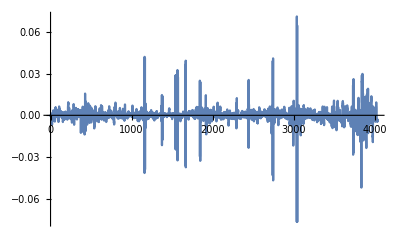

```mathematica
ListLinePlot[rsWethUsdc90dFiltered4Week, PlotRange->All]
```

```mathematica
edistWethUsdc90dFiltered4Week= EstimatedDistribution[rsWethUsdc90dFiltered4Week, StableDistribution[1, aWU90dF4W, bWU90dF4W, locWU90dF4W, scaleWE90dF4W]]
```

StableDistribution[1,1.42855,-0.0680586,0.0000962224,0.00156667]

```mathematica
rsWethUsdc90dFiltered6Week = Differences[Log[twapsWethUsdc90dFiltered6Week]]
```

{-0.00120673,0.000176452,-0.0000603568,-0.000373722,-0.000389599,0.000559858,-0.00092094,-0.00154871,-0.000905547,-0.000584311,-0.00172231,-0.00371162,-0.00218903,-0.00259613,-0.00374997,-0.00385087,-0.00499694,-0.00681335,-0.00674886,-0.00538641,-0.00238816,0.0014468,0.00178939,0.000805576,-0.0000377299,-0.00155115,-0.00338662,-0.00382918,-0.00321668,-0.00270154,-0.00132964,0.000186854,0.00248069,0.00193942,0.00361139,0.00131712,0.00210643,0.00262488,0.00257794,0.00174097,0.00254967,0.00294714,0.00224079,0.00201131,0.00100575,-0.00125599,-0.00167678,-0.00119665,-0.00236811,-0.00157824,-0.00332412,-0.00354818,-0.00450461,-0.00398038,-0.00322619,-0.00304323,0.000142204,0.000979734,0.0021921,0.00450208,0.00447003,0.00571894,0.00373655,0.00548546,0.00235632,0.00100711,0.00263737,0.000611337,-0.000136787,3.23868×10^-6,0.000777499,0.00199232,0.00303221,0.00327366,0.0033268,0.00307257,0.00216783,0.000783838,-0.000080765,0.000712625,0.000341638,-0.00024731,-0.00129321,-0.000717748,-0.0014396,-0.000834414,0.0000370664,0.000883407,0.00188126,0.00330856,0.0033331,0.00375294,0.00315136,0.000968898,-0.000801161,-0.00274671,-0.00394275,-0.00478984,-0.00467682,-0.00443888,-0.00235901,-0.000880246,0.00120961,0.00528268,0.00433957,0.00635964,0.00568107,0.00541609,0.00487764,0.00308507,0.00410442,0.00120017,0.00197393,0.00275295,0.00157799,0.00366619,0.00206488,0.00133458,0.000382621,-0.0000699762,0.00016049,0.00183379,0.00206868,0.00300834,0.00278611,0.00253281,0.00150304,0.0000776621,-0.000766576,-0.000219429,0.00062098,0.000245869,0.00224434,0.00260876,0.00210895,0.000646611,0.00125299,-4.26556×10^-6,-0.00153047,-0.00196873,-0.000776981,-0.000962884,0.00028361,0.0000302359,0.000690131,0.0000496851,0.00153279,0.00162621,0.00174437,0.000266823,-0.0012285,-0.00483641,-0.00409798,-0.00398706,-0.00134311,0.000485584,0.00229321,0.00220958,0.000161885,-0.0000742672,0.000928476,0.000205861,0.00101243,0.000866467,0.000885114,-0.000199799,-0.00127449,-0.00280245,-0.0033278,-0.00277031,-0.000607151,-0.00189991,0.000708547,0.000977043,0.00122085,0.000341527,0.000403759,-0.000586693,-0.000678702,-0.000395253,0.000632638,0.000902484,0.00103304,0.00270694,0.00160654,-0.000847635,-0.00119222,-0.00175055,-0.00249942,-0.00194127,-0.00137353,-0.0013237,-0.000759113,-0.000822173,-0.000615807,0.00114548,0.00105966,0.000674579,0.00162314,0.00101654,0.000823438,0.00060543,-0.000267887,-0.000910003,-0.00234046,-0.00258329,-0.00313232,-0.00231122,-0.00201389,-0.0022762,-0.00161991,-0.00147791,-0.0000243955,0.00067665,0.0060331,0.00668285,0.00927214,0.00797051,0.00902686,0.00389741,0.00219452,0.00210222,0.000445539,0.00103525,0.00128522,0.000247569,0.0011596,0.00361498,0.00495561,0.00529279,0.00420697,0.00408244,0.000438949,-0.000374359,-0.000597394,0.00204706,0.00254348,0.00195034,0.0000247282,-0.000905713,-0.00238829,-0.00181462,-0.000955324,-0.00165848,-0.00166356,-0.000448398,-0.0000418368,-0.000962198,-0.000526023,-0.000771889,-0.00113149,-0.00087899,0.000785294,0.00210836,0.00254428,0.00193499,0.000597359,-0.000959418,-0.00173637,-0.00221478,-0.0032536,-0.00200872,-0.00166366,-0.00528351,0.00228401,-0.000396164,-0.00140414,-0.00116982,0.00374935,-0.00420261,-0.00273237,-0.00157084,-0.00223279,-0.00405097,-0.00261365,0.000508622,0.00103635,-0.000164515,-0.0000628882,-0.000951101,-0.000162466,0.000665113,0.00251147,0.00592911,0.00806295,0.00596692,0.00549004,0.00330576,-0.000737829,-0.00550944,-0.00680145,-0.00387939,-0.00231952,0.000446972,0.00514113,0.0043007,0.00136402,-0.00100532,-0.00136694,-0.00138374,-0.00102386,0.000420436,0.00251006,0.00290296,0.00302551,0.00287687,0.00101647,0.00130164,0.0009427,0.00163272,0.00355894,0.00254027,0.00534872,0.00328251,0.000504665,-0.000189969,-0.000860302,-0.00234141,-0.00133308,-0.000212404,-0.000577845,-0.000651895,-0.000569861,-0.00188448,-0.00219684,-0.00299699,-0.00218893,-0.00093305,0.00102137,0.00148281,0.00397436,0.00296892,0.00417452,0.00277819,0.0021355,0.00139401,0.00222117,0.00218928,0.00276008,0.00360778,0.00444973,0.00416209,0.00330268,0.00318243,0.0027957,0.00224798,0.00145072,0.00158945,0.000651551,-0.00122243,-0.00100825,-0.0001823,0.0000705225,-0.000749663,-0.000746842,0.000326147,-0.000404649,0.00054826,0.00273891,0.00300199,0.00219743,0.00106368,0.000615812,-0.000113195,0.000718815,0.0022022,0.00261939,0.0036032,0.00383303,-0.000961861,-0.00216249,-0.00328255,-0.00409711,-0.0126016,-0.00504819,-0.00349995,-0.000706687,0.00103729,0.00136636,-0.00120346,-0.00338883,-0.00431124,-0.00296884,-0.00108496,0.0000695733,0.00142483,-0.0023581,-0.00553602,-0.00727636,-0.0092007,-0.0118317,-0.0107324,-0.00400684,-0.00258077,-0.000348289,0.00414171,0.00622641,0.00211121,0.000154442,0.000745415,-0.000588753,-0.00172617,-0.000141715,0.00208687,0.00152084,0.0015393,-0.000833912,-0.00201515,-0.00103073,0.000283345,-0.00115785,-0.00157559,-0.00214027,-0.00500302,-0.00799012,-0.00601438,-0.00694454,-0.00459589,-0.00846632,-0.0138003,-0.0127245,-0.00823448,-0.00693386,3.57542×10^-6,-0.00603135,0.0156081,0.00445268,0.0027864,0.00281029,0.0101999,-0.0114221,-0.000911608,-0.00357121,-0.0062516,-0.00219527,-0.00662301,-0.00450093,-0.000491038,0.00115676,0.000382632,0.00306648,-0.00141802,-0.00508591,-0.0033121,-0.00198609,0.000196775,0.00318695,0.00105543,-0.00314687,-0.00493772,-0.0062809,-0.00669001,-0.00197024,0.002545,0.00397548,0.00664627,0.00506877,0.00290276,0.000112059,0.000552199,-0.000258701,0.00278543,0.00554231,0.00672165,0.00870246,0.0058659,0.00278655,0.00256674,0.00239826,0.00237098,0.00120443,0.00266766,-0.000104853,-0.00174875,-0.00361806,-0.00177669,-0.00377022,-0.00261829,-0.00314037,-0.00395221,-0.00546506,-0.00215465,-0.00114284,0.00177262,0.00463417,0.00691103,0.00487133,0.00370479,0.00227567,-0.000406678,0.000569698,0.00289343,0.00389197,0.00468766,0.00583437,0.00210819,0.00231993,0.000128694,-0.000935311,-0.00134891,-0.000956703,-0.00512835,-0.00246365,-0.000600981,-0.000159904,0.00141108,0.00515938,0.00353114,0.00427087,0.00242524,0.00106617,0.00053809,0.000319866,0.00174101,0.00169106,0.00115526,0.00099856,-0.00089797,-0.00263275,-0.00228707,-0.000550966,-0.00118163,-0.00124948,-0.000957185,-0.00252525,-0.00283688,-0.00256824,-0.00164856,0.000120219,0.00140416,0.00139857,0.00220359,0.00216545,0.00178297,0.0033324,0.00215588,-0.00109466,0.00139342,-0.00942686,-0.00789698,-0.00787459,-0.00469481,-0.00744448,0.00384828,0.000848758,0.000367058,-0.00213207,-0.00301034,-0.00183259,0.000645233,0.000492977,0.00390305,0.00656524,0.00370489,0.00413998,0.00228553,0.000542292,-0.00167351,-0.000141523,-0.000404621,0.000174401,0.000815721,0.00153486,-0.000492745,-0.000207424,-0.000332305,-0.0000290578,0.000860051,0.00107633,0.00105768,-0.000115579,-0.00192669,-0.00277235,-0.0024697,-0.00431359,-0.00412185,-0.00118579,-0.000975521,-0.000461467,0.000589419,0.00163457,0.00169184,0.0014601,0.00180705,-0.000527823,-0.00163603,-0.00307266,-0.00280879,-0.00282746,-0.00119031,-0.00259338,-0.00269458,-0.00441814,-0.00421308,-0.00487301,-0.00384606,-0.0024068,-0.00116728,-0.00062649,-0.00235755,-0.001129,0.00020115,-0.000197578,-0.000657545,0.00420281,0.00501052,0.00178519,0.00206233,0.00162655,-0.000448803,-0.00122814,-0.000879599,-0.00228374,-0.00145558,-0.00227247,-0.000861159,-0.000950716,-0.00165397,-0.000283907,0.00123609,0.00278327,0.00346455,0.00732741,0.00421292,0.0022428,0.00119173,-0.000244369,-0.000938577,-0.000866448,-0.00315846,-0.00195881,-0.000822664,0.000449665,0.00176114,0.00654132,0.00442676,0.00273136,0.00219691,0.00225034,-0.000494392,-0.000455288,0.0000653734,0.000162442,-0.000293995,-0.00113959,-0.000445806,0.000559219,0.00113625,0.00165103,0.0023337,0.00167441,0.00038733,-0.000264483,-0.00014555,-0.000721203,-0.0013545,-0.00131775,-0.00148765,-0.00368341,-0.00255773,-0.00183317,-0.00110648,-0.00184839,-0.00357169,-0.00268691,-0.00135763,-0.00118826,-0.00259678,-0.000441151,-0.000689152,-0.00106823,-0.00101267,0.00155722,0.00191746,0.0023195,0.00228884,0.00135436,0.000287349,0.000402753,0.000133519,0.000359978,0.000207549,-0.000834001,-0.00217155,-0.00214295,-0.00421486,-0.00481491,-0.00414322,-0.00272072,-0.00224655,-0.00133937,-0.000807712,0.0002067,0.000593348,0.000970919,0.00145467,0.00165921,0.000482959,0.000376061,0.000136985,-0.000109334,-0.000126934,-0.000581944,-0.000879138,-0.00206599,-0.0018632,-0.00180305,-0.000997964,0.000552587,0.000589507,0.00114622,0.00215245,0.00119253,0.0027759,0.00384843,0.00323833,0.00188691,0.000715281,-0.00139645,0.00138431,0.0028638,0.00487441,0.00650475,0.00572486,0.00190231,0.000508831,-0.00163774,-0.00105941,0.000355478,0.000561101,0.0017383,0.00239054,0.00275324,0.00379113,0.00269575,0.00209498,0.00234747,0.000789187,0.000888326,0.00106607,0.0000390036,-0.0000525149,-0.0000821205,-0.000556964,0.000461147,0.00167898,0.00102753,0.00253293,0.00325176,0.00215814,0.00165608,0.000163246,0.000269869,0.000040018,-0.00118776,-0.000608973,0.000444086,0.000266682,0.0000139491,0.00115176,-0.000157003,-0.0018536,-0.00156399,-0.00143625,-0.00181795,-0.00172224,-0.000951319,-0.0027338,-0.00290476,-0.00252172,-0.00194732,-0.0004145,-0.000291751,0.000606317,-0.000385714,-0.00267611,-0.0025355,-0.00115107,-0.00132192,-0.00200004,-0.00457616,-0.00559553,-0.00429184,-0.00661355,-0.00646869,-0.00155098,0.000668081,0.000853597,0.00374922,0.00604024,0.00552838,0.00478614,0.00206674,0.00275674,0.00438478,0.00272398,0.00193095,0.00311733,0.00756794,0.00913441,0.00897017,0.00804286,0.0077439,0.00482622,0.00199162,0.00162826,0.00249967,0.00292999,0.00318709,0.00334572,0.000962092,-0.000387674,-0.000873219,-0.000166592,-0.000589148,0.00165579,0.00136832,0.000670425,-0.0000450499,0.000227281,0.00097717,0.00165013,0.00142033,0.000842973,0.000234833,-0.000560104,-0.00218888,-0.00153094,-0.000487778,0.0000201364,0.000171513,0.00236449,0.00259948,0.00211419,0.00243991,0.00193531,-0.000109346,-0.00162508,-0.00240107,-0.00241968,-0.00186829,-0.00116043,-0.000866059,-0.00110812,-0.0011947,-0.00158624,-0.00124399,-0.000265758,-0.000294621,-0.00092884,-0.000592053,0.00221002,0.00327831,0.00304925,0.00529694,0.00459602,0.00108425,0.000509407,0.00060931,0.00127141,0.0015676,0.00223282,0.00302034,0.00244967,0.000842439,-0.000652185,-0.000480236,-0.000902864,-0.00203126,-0.00120842,-0.00174557,-0.00179562,-0.000365795,0.000516376,0.000600133,0.000788552,-0.0000507764,-0.00205586,-0.000868774,-0.000639892,-0.000710718,-0.0000478221,0.000538015,0.000799382,0.00141177,0.000242582,-0.000230628,-0.00222298,-0.0016392,-0.00211303,0.00115072,0.00293122,0.00471373,0.00239054,0.00279118,0.000304917,-0.000603432,-0.00208368,-0.00169736,-0.00124682,-0.0012971,-0.000776473,-0.00064134,-0.000571684,-0.000610072,-0.000415267,-0.000689104,-0.0010389,-0.00104936,-0.00114247,-0.00389013,-0.00287061,-0.00345415,-0.00146925,0.000809617,0.00315623,0.00449341,0.0077896,0.00491217,0.00285559,0.00159224,0.00154276,-0.000965606,-0.000133131,-0.0000589046,0.000575507,0.00130704,0.00118483,-0.000446293,-0.000308394,-0.00101341,-0.00121398,-0.00184522,-0.000121873,-0.0000669166,0.000202302,0.000011791,0.0000613097,0.000877181,0.00092317,0.000681095,0.00102483,0.000978949,0.000449505,-0.000546981,-0.00178726,-0.0019691,-0.00237213,-0.00218041,-0.00175071,-0.000352776,0.000179633,0.000135227,0.000288145,0.000817332,0.00144868,0.0020547,0.00232534,0.00244505,0.00120557,0.00133906,0.00287408,0.00157919,0.00204595,0.00179106,0.00192126,0.000724835,0.000382512,0.000375168,-0.000228686,-0.000503744,-0.000898399,-0.000763558,-0.000607949,-0.000116725,-0.000199824,0.0000961991,-0.000569861,-0.000306774,-0.000210067,0.000307569,0.000141434,0.000924759,0.000448156,-0.000084335,-0.000202221,-0.00025325,-0.000526525,-0.000136104,0.000788527,0.000945125,0.00114049,0.00157497,0.00167556,0.00135261,0.00159875,0.000749986,0.0000842274,-0.000902854,-0.00104242,-0.00116856,-0.000918878,-0.000989948,-0.000842766,-0.0010209,-0.00102635,0.000980125,0.00466948,0.00435123,0.00699025,0.00655278,0.00483603,0.00138255,0.00181332,0.00206437,0.00261004,0.00139139,0.0026052,0.000192994,-0.000594479,-0.00191702,-0.000874915,-0.00177684,-0.00119709,-0.00118025,0.0000498224,-0.0000695999,-0.000173381,-0.000463836,0.000109768,0.000148284,-0.000310118,0.000274326,0.000552073,-0.00118885,-0.00203713,-0.00186567,-0.000657554,-0.000552606,0.000677591,0.00176288,0.00167314,0.000343884,0.000628297,0.000467979,-0.000348427,0.0006145,0.00054536,-0.000128062,-0.000416618,-0.000521026,-0.0015129,-0.00191137,-0.000968557,0.0000143828,0.00106242,0.00156105,0.00297838,0.00404862,0.00454336,0.00323331,0.00278779,0.00188643,0.00074969,0.000215854,0.000703627,0.00120311,0.0015477,0.00117297,0.00119751,-0.0000595017,-0.00130719,-0.00275445,-0.00369014,-0.00390995,-0.00416706,-0.00331629,-0.00267624,-0.00124081,-0.000435451,0.00023022,0.000462324,0.000644081,-0.000343244,-0.000732279,-0.000314967,-0.000838453,-0.0024047,-0.000602897,-0.00200062,-0.00429456,-0.00314678,-0.00368357,-0.000863389,-0.00298032,0.000781605,0.00146051,0.00267362,0.00156457,0.00253169,0.00152362,0.00112573,0.000719234,0.000428393,0.000405166,-0.000222705,-0.0015047,-0.00186106,-0.002133,-0.00157837,0.0000362676,0.000672393,0.00185016,0.00217979,0.00179423,0.0016508,0.00283524,0.00313298,0.00340067,0.00455065,0.00579742,0.00377328,0.00360246,0.00312079,0.00222869,0.00140936,0.000989776,0.00169525,-0.00242705,-0.00209561,-0.0018528,-0.00209557,-0.000946723,0.00186983,0.00171426,0.00196074,0.00149224,0.00033871,-0.00115616,-0.00189843,-0.00357131,-0.00211127,-0.00228,-0.000137593,0.000618353,0.00150091,0.00170323,0.00267142,0.00171991,0.00190605,0.00151379,0.00109552,0.000747929,-8.32535×10^-6,-0.0000696488,0.00123753,0.00114301,0.000810575,-0.0414512,0.0419846,-0.000682734,-0.0011462,-0.0000871902,0.041082,-0.0388866,-0.0086889,0.00695421,-0.000777239,-0.00195428,-0.00185956,0.00843883,-0.0090184,-0.0000178437,0.0012989,0.00316076,0.00380601,0.00280303,0.000709552,-0.000329469,-0.00221543,-0.00344843,-0.00155582,-0.000329168,-0.0000441934,0.000735073,0.00259507,0.00167799,0.00139987,0.00114346,0.00037167,-0.000835275,-0.00126008,-0.00214914,-0.00193602,-0.00151427,-0.00155432,-0.000963495,0.000344132,0.000623351,0.000445749,0.000462623,0.0000709405,-0.000302673,-0.000857178,-0.000336417,-0.000315789,-0.000821418,-0.00233291,-0.00191269,-0.0022671,-0.00199191,-0.000830382,-0.000560195,-0.0000881161,0.000826126,0.00100014,0.000773918,0.0017694,0.00187312,0.0014366,0.00149527,0.00126627,0.00209366,0.00110499,0.00131611,0.000622154,0.00024545,0.000265324,0.000329664,-0.000106138,-0.000108165,-0.00056995,-0.00112594,-0.000854892,-0.00109436,-0.00102154,0.00100342,0.00273074,0.00301677,0.0037619,0.00375775,0.00245633,0.000342655,0.000150083,-0.000116608,-0.000196338,0.000114894,0.000638325,0.000272947,0.0000955498,0.000132804,-0.000321559,-0.000631006,0.000643513,0.0013194,0.00149388,0.00202969,0.0021509,0.000318524,-0.00045603,-0.00101728,-0.00158425,-0.00245614,-0.00157256,-0.00106742,-0.000512263,0.000120067,0.000483341,0.000529602,0.000982815,0.00175016,0.00120714,0.00128144,0.00122909,-0.000382203,-0.00189347,-0.002069,-0.00248612,-0.00286884,-0.00371627,-0.00223168,-0.00119364,-0.00124053,0.00021558,-0.000951067,-0.00183928,-0.00191845,-0.00145192,-0.00188646,0.00106149,0.00129213,0.00103251,0.000932346,0.000880728,-0.0000126498,-0.0016209,-0.00262868,-0.00101439,-0.000917749,-0.00153729,0.0000288463,0.00102805,0.0000462368,-0.000223226,0.00117025,0.00220649,0.0026161,0.0029575,0.00270385,0.00283155,0.0017771,0.00154787,0.000945675,0.000489633,0.000191487,-0.0000167517,-0.00015439,-0.000620863,-0.00180333,-0.000406361,-0.00101402,-0.00116203,-0.00121671,-0.000429419,-0.00150654,-0.000298645,0.000396086,0.00096187,0.000640243,0.000714087,-0.000611885,-0.000655001,-0.000031475,-0.000359274,-0.000301282,0.000208999,0.00048424,-0.000402084,0.000406336,0.000705886,0.00111772,0.00102443,0.00121048,0.0012271,0.000721953,0.000623852,0.000554546,0.000440623,0.000299463,0.000211864,0.000377373,0.000588372,0.0011471,0.00120216,0.00130684,0.00136994,0.00061367,-0.0000851429,-0.0000897249,-0.000529571,-0.000431752,-0.000831333,-0.000470113,-0.000540893,-0.000233389,0.000474922,0.00121517,0.0012423,0.00687042,-0.00439132,-0.00022816,-0.000427838,0.0145414,-0.0214728,0.00490606,-0.000106052,-0.00109714,-0.0178032,0.0139376,-0.001578,-0.00204077,-0.00145424,-0.000911688,-0.000986064,-0.000957783,-0.00063972,0.000279193,0.000616705,0.000661391,-0.000181405,-0.000182426,-0.000452632,-0.000701488,-0.00100204,0.000828089,0.000936799,0.00119491,0.00142162,0.000730048,-0.0010337,-0.00064549,-0.000901503,-0.000834874,-0.0000124756,-0.000112099,0.0000744141,0.000335802,0.000209805,0.000403169,0.00145046,0.00136271,0.00110441,0.000845306,0.000787364,-0.0000138236,0.000380087,-0.0000181431,9.66408×10^-6,0.000179784,-0.0000714102,-0.000309686,0.000421643,0.00117555,0.00122649,0.00100583,0.000777633,0.000476592,-0.0000828325,-0.000651464,-0.000751128,-0.000666225,-0.000875066,-0.000950376,-0.000825752,-0.00130323,-0.000730362,-0.000554217,-0.000474488,-0.000175335,0.000199862,-0.00040209,-0.000365556,-0.00054007,-0.0000890267,-0.000144091,0.000480641,0.000898759,0.00121699,0.0013267,0.00146877,0.000785515,0.000415181,0.000110056,-0.0000248417,-0.000334675,-0.000252165,-0.000479,-0.0000305659,0.000414973,0.00384283,0.00464208,0.00459038,0.00368655,0.00497468,0.000773252,1.38813×10^-6,-0.000248345,0.000728654,0.000632891,0.000806726,0.00112336,0.000978499,0.000167927,-0.0000516025,-0.000132285,-0.000172418,-0.0000546051,0.00107165,0.00164232,0.00173899,0.00117991,0.00128991,-0.000548989,-0.000770046,-0.00104571,-0.000414962,0.00026135,0.000389526,0.000108301,0.0000929041,-0.000114462,-0.000323705,-0.000126862,0.000330517,0.000496064,0.000213113,-0.000167446,-0.00139237,-0.00272959,-0.00232198,-0.00172782,-0.000684152,0.000231279,0.000995399,0.00050165,-0.000188684,-0.000769504,-0.0000244679,0.00099389,0.00124882,0.00156672,0.00141812,0.00113295,0.000454937,0.000420587,0.00130814,0.00155827,0.00131251,0.00135534,0.000837613,0.000137285,-0.000387778,-0.000451854,-0.000511923,-0.000313462,-0.00010025,-0.0000708208,-0.000263446,-0.000140434,-0.000482702,-0.000815066,-0.00112947,-0.000797436,-0.00134519,-0.000575632,0.000204589,0.00166638,0.0016478,0.00242032,0.00200975,-0.024293,0.0287025,0.00241599,0.00262571,0.00247084,0.0287808,-0.024599,0.00101865,0.00101533,0.000728176,0.000305472,0.000195423,0.000356933,0.000212255,-2.8602×10^-7,-0.000239674,-0.00103511,-0.00132637,-0.000243642,-0.000486028,0.000372106,0.00153891,0.0017067,0.00118684,0.0325148,-0.0323952,-0.00123801,-0.00107113,-0.000947338,-0.0272633,0.0274025,0.000942134,0.000724385,0.000939389,0.000352002,0.000550232,0.000914905,0.000628839,0.000935858,-0.00011343,-0.000281164,-0.000675134,-0.000591396,-0.000761658,-0.000398219,-0.000572141,-0.000255126,-0.0000255528,0.0000943235,0.00038541,0.000760633,0.00123961,0.000831282,0.000754185,0.000779138,0.000484623,0.0000428802,-0.000424447,-0.00208702,-0.00246332,-0.0039297,-0.00428938,-0.000577303,0.000242626,0.0000245399,0.000825934,0.00105264,-0.0000251619,-0.000716084,0.000179684,0.000199738,0.000297906,0.000168538,0.000115773,-0.000192196,-0.000645087,-0.00193845,-0.00193054,-0.00152017,-0.00167191,-0.00107768,-0.00121486,-0.00119745,-0.00173691,-0.00161948,-0.000748798,0.000209102,0.000428268,0.000734845,0.000650775,0.00106822,0.00124182,0.00227413,0.00236237,0.00269409,0.00165144,0.00127944,0.000140168,-0.000212721,-0.000154803,-0.0000187387,0.00024798,0.000754791,0.00119451,0.00112729,0.000954665,0.000378853,-0.000311067,-0.000222788,-0.000307194,0.0000524551,-0.00049898,-0.000822251,-0.000462705,-0.000779924,-0.000648556,0.0000669315,0.000405771,0.000312875,0.000132004,-0.0000905182,-0.0359786,0.0363046,0.000719188,0.000887844,0.00099192,0.0392383,-0.0373389,0.000206924,0.000342924,0.000147036,-0.0000812063,-0.0000587938,-0.000010622,0.0000676669,0.000470984,0.000573227,0.000683607,0.000486529,0.00116536,0.00137443,0.00126916,0.00221239,0.00210869,0.00136684,0.00111328,0.000556192,4.68688×10^-6,-0.000322991,-0.000525033,-0.000536487,-0.000511655,-0.000431705,0.000109535,0.000572768,0.000679499,0.000717861,0.0000733799,-0.0012067,-0.00178257,-0.00263177,-0.00309087,-0.00156029,-0.000561773,0.000348814,0.000448087,0.000741062,0.00179748,0.00209749,0.00311744,0.00242346,0.00295951,0.00106534,0.000726196,0.000531729,0.000642593,0.00207244,0.00198173,0.00145474,0.00181094,0.00119526,-0.0000490975,0.000415406,0.000611772,0.0014115,0.00154647,0.00167922,0.00156765,0.00175257,0.00165708,0.00100607,0.000475822,0.000133392,-0.000329116,-0.000433984,0.000604679,0.000488353,0.00172646,0.00300421,0.00327459,0.00199304,0.00110795,0.000996769,0.000117901,-0.000265054,-0.00057575,-0.000449893,0.000990467,0.0032076,0.00328159,0.00294208,0.00378181,0.00268727,0.00198293,0.00258181,0.00321178,0.00243213,0.00144033,-0.00101848,-0.00100298,-0.00112721,-0.000910306,0.000869275,-0.000377356,-0.00103542,-0.00152943,-0.001569,-0.00207574,-0.000185879,0.000708944,0.00165033,0.00164907,0.00174654,0.000590943,0.0000731581,-0.000917137,-0.00171684,-0.0026487,-0.00158419,-0.000924789,-0.00157356,-0.000800716,-0.000225496,-0.00233173,-0.00216651,-0.00138314,0.000223727,0.000821374,0.00270273,0.00422558,0.0033642,0.00176459,0.0024482,0.00168429,-0.0000629361,0.0000132796,0.00049209,-0.000300669,-0.000369268,0.00319694,0.00566947,0.00476461,0.00604239,0.00532524,0.00430516,0.0013428,0.00152603,0.00288647,0.00176983,0.00150136,0.00240793,0.00248646,0.00171193,-0.0000785452,-0.00165977,-0.000715552,-0.00111037,-0.00223867,-0.00109765,0.000818495,-0.00133836,-0.00203,-0.00011995,-0.0000860915,-0.000128324,0.0000563381,0.00117238,-0.000158133,0.00174783,0.00287387,0.00584965,0.00576358,0.00558716,0.00394461,0.00241308,0.0021106,0.00192353,0.00317306,0.00338297,0.00283384,0.0248727,-0.0295747,-0.00383283,-0.00312703,-0.00851689,-0.0327107,0.0239553,-0.00499594,-0.00491803,0.000593634,0.000786451,-0.00052929,-0.00289306,-0.0028111,-0.00220873,-0.00387005,-0.00423728,-0.000974656,-0.00045358,-0.00038493,0.00121984,0.000662481,0.000182991,0.00262872,0.00301494,0.00350616,0.00492893,0.00553839,0.00516567,0.00351876,0.00380111,0.00157244,0.00209146,0.00120385,0.000637409,0.000924354,0.00113682,-0.00025714,-0.00181377,-0.000730396,-0.000974799,-0.0012416,-0.00135503,-0.00119148,-0.00260131,-0.0040644,-0.00282087,-0.00174289,-0.00176069,-0.0014499,0.00222433,0.00218297,0.00380129,0.00368075,0.00269203,0.000260497,0.00085787,0.00160457,0.00182732,0.00401232,0.00475679,0.0026052,0.00121174,0.00205306,0.00300466,0.00256725,0.00305798,0.00237677,-0.0000541018,-0.00173103,0.000212214,-0.000311547,0.0023477,0.00313266,0.0144512,-0.00821527,-0.000233259,0.00056875,-0.0024141,-0.0136794,0.000907223,-0.00482629,-0.00769023,-0.00747064,-0.0072335,-0.00919936,-0.00783773,-0.00282945,-0.000552179,-0.0033097,-0.00492109,0.00136816,0.00209213,0.000817307,0.00210796,0.00522972,0.00402665,0.00189449,0.00252173,0.00251411,0.00316717,0.00382487,0.00245615,0.00212261,0.0024164,0.00348178,-0.0012568,0.00252062,0.00374274,-0.000014624,-0.0039969,0.00190518,-0.00181569,-0.00222069,0.000102459,-0.000351699,-0.00275528,-0.00307612,-0.0030861,-0.00445619,-0.00588402,-0.00278822,-0.00537252,-0.00111003,0.00106573,0.00149643,0.00119183,-0.00123869,-0.00321451,-0.00172741,-0.000772273,0.000197519,0.00399308,0.00389842,0.00285734,0.00352615,0.00349761,0.00249881,0.00279715,0.00276691,-0.000309147,-0.0000601254,-0.00173293,-0.00264434,-0.00202092,-0.00361974,-0.00439218,-0.00228394,-0.00179277,-0.00031246,-0.00038357,0.000503898,0.000934868,-0.000200978,-0.00243319,-0.00339921,-0.0025272,-0.00178304,0.0001005,0.000836132,0.000904455,0.0000406236,-0.00189845,-0.00266516,-0.00164924,-0.000771383,0.000356698,0.00163991,0.00280642,0.0033015,0.00506714,0.00617555,0.00352987,0.00374607,0.00350605,0.00078303,0.000772759,-0.000500961,-0.000762605,-0.000359629,0.000727157,0.00293034,0.00263243,0.00132018,0.000951084,-0.000238197,-0.00100745,-0.00100096,-0.000407248,-0.000553453,-0.000566249,-0.00122448,-0.000856886,0.000767422,0.00107443,0.000781722,0.000444886,0.000863504,-0.0000132857,-0.0000705493,0.000532784,0.00019341,0.000572388,-0.00114746,-0.00275928,-0.00435216,-0.00310706,-0.00183402,-0.000973186,0.000272731,0.00229309,0.000305783,-0.00208151,-0.00127732,-0.00143341,0.00060919,0.00394767,0.00593063,0.00555928,0.00908481,0.00489599,0.000869042,0.000140593,-0.00129995,-0.00165116,-0.00130949,-0.000303588,0.000118218,0.000053444,0.000206294,0.000918342,0.0014481,0.00173472,0.00290892,0.00244765,0.00315486,0.00174062,0.000488073,-0.0000586091,-0.00072441,-0.000917125,-0.000931368,-0.000178295,-0.00044664,-0.00179015,-0.00106988,-0.0007553,0.00152118,0.00273696,0.00596415,0.00310268,0.00628376,0.00189893,0.00125276,0.0012417,0.000266079,0.000119,-0.000399568,-0.0026541,-0.00267646,-0.00294734,-0.00256812,-0.00296245,-0.000972359,-0.000784195,0.000433367,0.000449396,0.000833865,0.00141228,0.00145332,0.000960328,0.000277953,0.000356543,-0.000698253,-0.00125817,-0.0014724,-0.00142044,-0.00110298,0.000240717,0.00129456,0.00120847,0.000966442,0.000170251,-0.00159325,-0.00239753,-0.00292885,-0.00194492,-0.000483647,0.000182052,-0.0000638852,0.000100221,-0.00174082,-0.00210883,-0.002491,-0.00265718,-0.000560939,-0.00164701,0.000912033,0.00131577,0.00239785,0.00196796,0.000937242,0.00184442,0.000563325,-0.000281282,-0.0003534,0.0000597015,-0.0000772389,0.000292661,0.000948287,0.00142395,0.00225833,0.00222131,0.00188461,0.00242533,0.00105813,0.000187083,-0.0000600749,0.000975249,0.00113938,0.00180085,0.000946857,0.00114737,-0.000210155,-0.000959771,-0.00196903,-0.000861534,-0.00137392,-0.000989096,-0.000269792,-0.000205979,-0.00056322,-0.0000886163,0.000523963,0.000747396,0.00156284,0.002812,0.00403125,0.00420561,0.00305489,0.0026046,0.0026826,0.00216038,0.00138547,0.00037401,0.000164857,-0.000396506,-0.000152172,-0.000405843,0.00075872,0.00123945,-0.00119557,-0.00236066,-0.00348023,-0.00742075,-0.00638938,-0.00552759,-0.00632436,-0.00490086,0.000445711,0.00224257,0.00044313,0.000962127,0.00105827,0.000109169,-0.00176864,0.000528903,0.00105145,0.00179383,0.00188006,0.00225211,0.00346089,0.00214399,0.00182764,0.00121772,0.00178012,0.000750892,0.000115139,-0.00102114,-0.00105887,-0.00204081,-0.00130553,-0.00222239,0.000904083,0.00067629,0.000316059,0.0010496,0.00126945,-0.00173688,-0.0019298,-0.00140729,-0.00251237,-0.00263919,-0.00127105,-0.000808188,-0.00146364,-0.00240915,-0.00179925,-0.00134519,-0.00153975,-0.00251534,-0.000622866,-0.0000259539,0.00012354,-0.0015684,-0.00266209,-0.00160165,-0.00256147,-0.00241131,-0.000363001,0.00161748,0.00078649,0.00110791,0.000866885,0.00108138,0.000162328,0.0010794,0.00177136,0.001546,0.0014765,0.00160927,0.000947748,0.00126002,0.00149442,0.00133562,0.000758814,0.000371539,-0.00137651,-0.00275927,-0.00281483,-0.00161339,-0.00142326,0.000470589,0.00182062,0.00120511,0.000949182,0.00184013,0.000820049,0.000916946,0.00138055,0.0012242,0.000783834,0.000258211,-0.00020784,-0.000529016,-0.00145782,-0.00050066,-0.000242408,-0.000190726,-0.000272342,0.00870858,-0.00938654,0.000226467,0.00135186,0.00214189,-0.00558612,0.0123582,0.00198154,0.00187331,0.00122904,-0.0000327771,-0.00035231,-0.000111837,-0.000915632,-0.000997477,-0.000817405,0.000491048,0.00123543,0.00144688,0.00131865,0.00367408,0.00318396,0.00290532,0.00326777,0.00201464,-0.0000197004,-0.000629549,-0.000354688,-0.000946516,-0.0000744153,0.000214734,0.000136544,-0.00138458,-0.00130297,-0.0014537,-0.00235215,-0.00113789,-0.000956286,-0.000715695,0.000167683,-0.000073345,-0.000781932,-0.00012715,-0.000326733,-0.0000108687,0.0000767404,0.000173384,-0.000711396,-0.0012155,-0.00227612,-0.00243543,-0.00215559,-0.000922316,-0.000348188,-0.000290524,0.000726065,-0.000702798,-0.00244335,-0.00241417,-0.00233529,-0.00204962,-0.000221369,0.000695697,0.00200261,0.00207223,0.00156893,0.000963892,0.00233496,0.00198935,0.00191329,0.00198049,0.00314483,0.00156601,0.00176995,0.0018349,0.00123532,0.000750063,0.000336193,-0.000201788,-0.000216785,-0.000988652,-0.000419541,-0.000342167,-0.000324196,-0.00025111,-0.0000132486,0.000464382,0.00106447,0.00229792,0.00252569,0.00188461,0.00230348,0.000165081,-0.00134994,-0.00134233,-0.00138248,-0.00167441,-0.000700946,-0.000438212,-0.000686447,-0.000712215,-0.00105928,-0.00109578,-0.00115833,-0.000922738,-0.00034599,0.0000328899,0.000453181,0.000697285,0.000964933,0.00152266,0.00269632,0.00215501,0.00176827,0.00118732,0.000169883,-0.00119999,-0.00131288,-0.000686424,0.0000260782,0.00124491,0.000539515,0.000311995,-0.000187368,-0.000784801,-0.00207383,-0.000995677,-0.00101084,-0.0000379421,0.000276334,0.00033208,0.0000498205,-0.000153706,0.000251057,0.000246037,0.00104269,0.000825627,0.00198544,0.00221282,0.00370657,0.00465255,0.00441804,0.0044784,0.00335551,0.00204703,0.00128545,0.0236239,-0.0215814,0.000892626,0.000817945,-0.00117677,-0.0233726,0.0254088,0.00361556,0.0047141,0.00714728,0.00766327,0.00370497,0.00421835,0.00393937,0.00100869,0.0014745,0.00237419,0.0000646105,-0.00015627,0.00108099,0.000278548,-0.0000291993,0.00106556,0.0000903253,-0.000506416,-0.00157183,-0.0013831,-0.000763981,0.00140743,0.000602496,0.00276716,0.00138255,0.00232088,0.000682154,0.00162766,0.00225019,0.00188019,0.00392805,0.00338308,0.0030612,-0.000705611,-0.000385554,-0.0017754,-0.00319005,-0.00267427,0.000512272,-0.000435567,-0.000113828,0.00120623,0.0016704,-0.000715668,-0.00242049,-0.00183339,-0.00126282,-0.00125467,0.000407135,0.0015933,0.00175303,0.00124896,0.000403527,-0.000606446,-0.000661656,-0.000364083,-0.000254914,0.00174212,0.0036066,0.0017302,0.00451918,0.000997394,-0.000733089,-0.0042658,-0.00273139,-0.00420842,-0.00085423,-0.000557168,0.00314565,0.00322806,0.00250835,0.00243235,-0.000375633,0.00180796,-0.000103922,0.00100169,0.00191945,0.00331461,0.00134777,0.00182497,0.00126491,-0.000521047,-0.000546575,-0.000765188,-0.000416963,-0.000959378,-0.000196021,0.000311696,0.000011184,-0.000925916,-0.000788498,-0.00121187,-0.00161215,-0.00191696,-0.00235332,-0.00170838,-0.0013512,-0.00292752,-0.000866122,0.000148203,-0.0000527912,0.000488796,0.00241671,0.00195636,0.000391473,-0.000634509,-0.0030682,-0.00461453,-0.00562987,-0.00574786,-0.00395106,-0.00575187,-0.00301677,-0.00101727,-0.000216769,-0.000565215,0.00251556,0.00259675,0.00240703,0.00119602,0.00255558,0.000341218,0.000856417,0.000939393,0.000994681,0.00108959,0.000631373,0.000108611,0.00310639,0.00578177,0.00463369,0.00452327,0.00256766,0.00471106,-0.00114186,-0.00191168,-0.000611302,-0.00100102,-0.00146098,-0.000238634,0.000842705,-0.000315055,-0.00031333,-0.000282625,-0.000738144,-0.00131135,-0.00100081,-0.00208771,-0.00134235,-0.00202946,-0.00121401,-0.000803067,0.000452666,0.000740171,0.00247809,0.00265119,0.00144515,0.00184186,0.00125848,0.000535616,-0.00035696,-0.000717763,-0.0000610798,-0.000417636,-0.000681036,-0.000797218,-0.00117583,-0.000650891,-0.00085598,-0.000160922,0.00130905,0.00124251,0.00110633,0.0013262,-0.000175301,-0.0000557503,-0.0000327326,-0.000447892,-0.000415711,0.0000310041,-0.000182795,-0.000139455,0.000845647,0.00174948,0.00279644,0.00244637,0.00205889,0.00100013,0.00161089,0.00181966,0.0027553,0.00331626,0.00422831,0.00427503,0.00399188,0.00200455,0.00102983,0.000241927,0.0011946,0.00172244,0.00352927,0.00394011,0.00279795,0.00113099,0.000940975,-0.0011495,0.000495932,0.00154998,0.000696839,0.000684924,0.000102126,-0.0000285485,-0.000765382,-0.000223431,0.000210089,0.000229674,-0.000641258,-0.00151659,-0.00155679,-0.000283917,-0.000575071,0.00154862,0.00308322,0.00249295,-0.000417872,-0.00032013,-0.0014582,-0.00188816,-0.00202631,-0.000378977,-0.00151651,-0.00175452,-0.00323786,-0.00241388,-0.0021879,-0.00476601,-0.00078802,0.0013701,0.00208239,0.00292734,0.00473306,0.00258072,0.00341433,0.00293841,0.00161016,0.00110754,0.00075209,0.000743838,-0.000459884,-0.00151989,-0.000963727,-0.00169915,-0.00166488,-0.00406685,-0.00242866,-0.00102321,0.000462844,0.00169653,0.0031999,0.00385124,0.0063698,0.00358053,0.00312746,0.00199671,-0.00046116,-0.000967721,0.000319938,-0.000445603,-0.00150406,-0.000382126,-0.00120701,-0.00185782,-0.00202129,-0.00176551,-0.000315822,-0.000267255,-0.000398202,-0.000446857,-0.00160282,-0.00324874,-0.00687208,-0.0114233,-0.0131474,-0.00872032,-0.00944447,-0.00726624,0.00128743,0.00463458,0.0044916,0.00401219,0.00689221,0.00586108,0.00237135,0.00318374,0.00197924,-0.0431046,0.0390679,-0.00306881,-0.00351551,-0.00252025,0.0408835,-0.0467432,0.000516683,0.00303111,-0.000471053,-0.00252701,-0.00314271,-0.00451802,-0.0059994,-0.00304083,0.00107092,0.00111775,0.000753468,0.000747164,-0.00217302,-0.00372884,-0.00345263,-0.00288786,-0.00551365,-0.00175151,0.000771507,0.000738079,0.00184446,0.00436616,0.00385479,0.00186312,0.00319401,0.00203679,0.00197918,-0.000575312,-0.00117265,-0.000630198,-0.000903144,-0.000797383,0.00219091,0.00333752,0.00319509,0.0037046,0.00157804,0.00140955,0.000654153,-0.000102,-0.000152606,-0.000127394,-0.000834521,-0.000969571,-0.00137292,-0.000770818,-0.00118365,0.00144451,0.000881575,0.00217271,0.00382645,0.00370432,0.00556962,0.00559227,0.00484759,0.00226277,0.000895377,0.000497512,-0.000507832,-0.00131686,-0.0035246,-0.00416264,-0.00433248,-0.00710977,-0.00272855,-0.00269022,0.000494129,-0.000657687,0.0013556,-0.00218052,-0.000393093,-0.00040081,0.00084422,0.00246397,0.0022899,0.00135281,0.0018224,0.00120686,0.00172933,0.00299156,0.000626934,0.00225426,0.0035895,0.00292705,0.000780448,0.00028198,0.000224904,-0.00157309,-0.0021576,-0.000769706,0.000892885,0.000727481,0.000996527,0.00183727,0.00255925,0.00298601,0.0010722,0.00073538,-0.00111639,-0.00145638,-0.000864915,-0.00030355,-0.000502376,0.000530638,0.00193243,0.00165203,0.00360191,0.00301757,0.00419381,0.00274433,0.00172849,0.00158611,-0.00140561,-0.000716547,-0.00132739,-0.000854923,-0.00114909,0.00126818,0.000169951,0.000810854,0.00103399,0.000782079,0.0010466,0.00147509,0.00248377,0.00103294,0.00161506,0.000752151,0.000532776,0.000338183,0.000143332,0.0000821191,0.000444562,0.000482955,0.00114415,0.00234907,0.00613053,0.00258967,0.00399015,0.00288587,0.00130712,0.00111167,0.00376849,0.00304652,0.00235773,0.00282257,0.000479958,-0.00203771,-0.00140483,0.0000409561,5.20711×10^-6,0.00180115,0.00156175,0.00192234,0.00121361,-0.000245605,-0.000016537,-0.000307849,-0.000809206,-0.00241167,-0.000679065,-0.000409587,-0.000590423,-0.000594187,-0.000122605,-0.0014611,-0.00136428,-0.000940374,-0.000159816,-0.000320865,0.000602151,0.000967899,0.0000614906,0.000943532,-0.000656577,-0.00141294,-0.000777211,-0.00131942,-0.00297842,-0.00211374,-0.00119521,-0.000555125,-0.000421001,0.000671624,0.00109152,0.000978963,0.000217364,0.00133626,0.00154898,0.00156341,0.00150007,0.0016137,-0.000682324,-0.00142841,-0.000313545,-0.000138334,-0.000588738,0.00191029,0.00541468,0.00246634,0.00132462,-0.00112034,-0.00659969,-0.00665327,-0.00469348,-0.00462223,-0.00543413,-0.00668797,-0.00344674,-0.00405872,-0.00311758,0.000994651,0.000660955,0.0012482,0.00193569,-0.000102633,-0.00165864,-0.00268709,-0.00471732,-0.0063195,-0.00530641,-0.00739477,-0.00651435,-0.00304174,-0.000326511,0.00143473,0.00250998,0.00655709,0.00305114,0.00285695,0.00182896,0.00182795,0.000235706,0.000704357,0.00229137,0.00202275,0.00135187,0.000376125,0.0000939089,-0.0032044,-0.00267939,0.00111095,0.00240522,0.00139676,0.000669726,-0.0025548,-0.00846334,-0.0217538,-0.0179602,-0.0108518,-0.00497106,-0.00201781,0.0104636,0.00864586,0.00530104,0.00223092,0.00112522,0.00143847,0.0035509,0.00301926,0.00366217,0.00226284,0.00167482,0.000279401,-0.00212451,-0.00437498,-0.00345323,-0.00393841,-0.00608562,-0.00193086,0.00146509,0.00157166,0.00192535,0.00144813,-0.00137283,-0.00169079,0.000115295,0.00152568,0.00345993,0.00476635,0.00303599,0.0029058,0.000753092,0.000299177,-0.000341567,0.000713456,0.000540374,-0.000102389,-0.000258049,-0.00100206,-0.0765007,0.0709871,-0.003102,-0.00348344,-0.00289519,0.0645426,-0.0765458,-0.00519438,-0.00712906,-0.00700444,-0.00830814,-0.0056229,-0.00158403,-0.00211745,-0.0026835,-0.00188717,-0.00649491,-0.00687884,-0.00240062,0.000469467,0.0032547,0.007401,0.00374015,0.00570024,0.00369844,0.00229917,0.00411626,0.00495161,-0.00107692,0.000916972,0.00284912,0.00205094,0.00274888,0.00510416,0.00382927,0.00144796,0.000134145,-0.00378137,-0.00402965,-0.0044768,-0.00510917,-0.00487584,-0.00047095,0.00161252,0.00273449,0.00301693,-0.00303826,-0.00567475,-0.0103864,-0.0143845,-0.0112564,-0.0032325,0.00231943,0.00133703,0.00393365,0.00126319,-0.00303508,-0.00577171,-0.00356748,-0.00040576,0.00343893,0.0045409,0.00372612,0.00158356,0.00155874,0.00028293,0.000503884,0.00200959,0.00353925,0.00252032,0.00416892,0.00389324,0.000770689,0.00261926,0.000265704,-0.00305518,-0.00254854,0.00050893,-0.000764466,-0.00456579,-0.00367366,-0.00345073,-0.00628002,-0.00284138,0.0020431,0.00663381,0.00631782,0.00736172,0.00501801,0.00454952,0.00469582,0.00360447,0.00522654,0.0031667,0.00434868,0.00248678,0.00037572,-0.00255347,-0.00277154,-0.00205307,-0.00259411,-0.00250334,-0.00183907,-0.000266025,-0.00015759,-0.00160732,-0.000530233,-0.0000701318,0.000628353,-0.000315424,-0.00053244,-0.000580903,-0.000459393,-0.000853975,0.000307399,0.00171647,0.00156007,0.00279797,0.00259728,0.00138853,0.00134688,-0.00115621,-0.00220481,-0.00182818,0.000119961,0.00226959,0.003237,0.00381047,0.00294356,0.0015041,0.00148385,0.00043021,0.00182352,0.00274522,0.00207818,0.00296379,0.00518892,0.0036671,0.000932159,0.00126076,0.00124577,0.0000477853,-0.000997273,0.0000689207,0.00045122,0.00252352,0.00150432,0.00351158,0.00209825,0.0017178,0.00083413,-0.000817183,-0.0017431,-0.000965603,-0.00163982,-0.000857379,-0.000258476,0.000382042,0.00014946,0.0013217,0.00339416,0.00281431,0.00351381,0.00267464,0.00241484,0.000952909,0.00296019,0.00436844,0.00499129,0.00377478,0.00240182,0.00190585,0.00114068,-0.000311426,-0.00177759,-0.000613357,-0.00108452,-0.00155347,-0.00066611,0.00090984,-0.000665187,-0.00120254,-0.000827022,-0.00125119,-0.00243069,-0.000980683,-0.00177361,-0.00179458,-0.00179767,-0.000848973,-0.00102348,-0.00154499,-0.000132447,-0.000501414,-0.00335928,-0.00192999,-0.00245018,-0.00318955,-0.00184202,0.00111802,0.000471414,0.00199844,0.00185081,0.000911288,0.00326148,0.00371215,0.00207214,0.00220905,0.00279781,-0.0000162399,-0.000519173,0.000289988,0.000615228,0.00103731,-0.000994275,-0.00085735,-0.00111702,-0.00370561,-0.00354121,0.000858927,0.000491353,0.00300091,0.00416512,0.00234769,0.000603737,-0.0000990471,-0.000901085,-0.00106502,-0.000807645,-0.00214311,-0.00167113,-0.00241754,-0.00240826,-0.00132903,-0.000886633,-0.000378445,-0.000127227,0.0000153536,-0.000838293,-0.00137286,-0.000954473,-0.00131831,-0.00222633,-0.000826916,0.000848426,0.000998269,-0.000333162,-0.000105496,-0.00300514,-0.00307191,-0.0036866,-0.00496553,-0.00295162,-0.00251192,-0.00135539,-0.000565257,-0.000128738,-0.000685878,-0.00211085,-0.00120627,0.00111883,0.000895134,-0.00110973,-0.00112977,-0.000857701,-0.00248178,-0.00387441,-0.00257546,-0.00192856,-0.00346471,-0.00180692,-0.000412821,0.00203265,0.00196333,0.00185042,0.00195252,0.00129879,0.00085586,0.000816525,0.00240196,0.00163193,0.000720071,0.00194503,0.00132978,-0.00114616,-0.00103216,-0.000925884,-0.00145687,-0.0030368,-0.00171236,-0.000924475,0.000451888,0.000368848,0.0024377,0.00193284,-0.000253045,-0.00215685,-0.00362106,-0.00477032,-0.00620824,-0.0056714,-0.00597,-0.00403952,-0.00506661,-0.00120769,0.000616,-0.0000748849,0.000636511,0.00120614,0.000402503,-0.0010665,-0.000612534,8.81797×10^-6,-0.00142961,-0.00421423,-0.00415535,-0.0015742,-1.58351×10^-6,0.00242286,0.00493679,0.00636397,0.00380818,0.00301539,0.00187698,0.00169833,0.0000693187,0.000278304,0.000229318,-0.000113309,0.000295962,0.000860387,-0.00172306,-0.0013973,-0.00276428,-0.00440553,-0.00600531,-0.00521368,-0.00707499,-0.00491131,0.000618539,0.00462289,0.00588932,0.00610781,0.00614198,0.00303878,0.0017082,0.00167093,0.00410719,0.00293797,0.000775657,0.000260551,0.000809935,0.0000185226,-0.000170375,-0.0000648231,-0.000371286,-0.00174124,-0.00184107,-0.00138345,0.000178139,0.000103539,0.00137432,0.0012075,0.0011016,-0.00118997,-0.000675284,-0.000791905,-0.00083646,-0.00118927,-0.00124388,-0.00062581,0.00225107,0.00392623,0.00585602,0.00335034,0.00224209,-0.000115511,-0.000458037,-0.00288052,-0.000694869,-0.00133256,-0.00197512,-0.000969326,-0.00143925,-0.00318013,-0.00070504,-0.00131062,-0.000696028,0.000364799,0.00122889,0.000744277,0.0012502,0.00123405,0.000963555,0.00113122,0.000668895,0.00125827,0.000922126,-0.000160994,-0.000560626,-0.00120987,-0.00261456,-0.00167861,-0.00252003,-0.00159631,-0.00296831,-0.00403952,-0.00508071,-0.00416874,-0.0031851,-0.00482031,-0.00046725,0.00044441,0.00053714,0.000751926,0.00102937,-0.00149586,-0.00176711,-0.00219302,-0.00317504,-0.00302904,5.3488×10^-6,-0.00150602,-0.00197874,-0.00258212,-0.000251319,-0.00193912,-0.00420099,-0.00415169,-0.00239672,-0.00640736,-0.0079819,-0.00322179,-0.000745239,0.0015169,0.00543087,0.006269,0.00237022,-0.00102789,-0.00226014,-0.00646222,-0.00921246,-0.00652922,-0.00294228,-0.00620415,-0.0055756,-0.00228907,-0.000625445,-0.00407098,-0.00273808,-0.00125474,-0.00267084,-0.00320623,-0.00301531,-0.00210383,0.00359545,0.0063142,0.00603667,0.0090433,0.0105832,0.00545775,0.00243829,0.00283138,0.000164947,-0.00126861,0.000963606,0.00185323,0.0013966,0.00211184,0.00145558,-0.00160105,-0.00137989,-0.00129492,-0.00468102,-0.00474567,-0.00843344,-0.00533229,-0.00864414,-0.00494021,-0.00156167,0.000944978,0.000844955,-0.000877415,-0.0013653,-0.00167225,-0.00330944,-0.00480853,-0.00662076,-0.00618197,-0.00552854,-0.0107244,-0.00913056,-0.00109297,0.000775361,0.000858686,0.00637875,0.00520756,0.00140619,-0.000605907,-0.00089435,-0.00377315,0.00400231,0.00836688,0.00673697,0.0104089,0.0097896,0.00166502,0.000488681,0.00398377,0.00315596,0.00544089,0.00583686,0.00305673,0.00298475,0.00379452,0.00174301,0.00182598,0.00105466,-0.0000490666,-0.00271694,-0.00163343,-0.00246362,0.000070479,0.00013034,-0.000755128,-0.000879518,-0.00223331,-0.00403671,-0.00256857,0.000480722,0.00048287,0.00203597,0.00361458,0.00387546,0.00183948,0.0000181126,-0.0026905,-0.001919,-0.00310032,-0.00312641,-0.00298603,-0.00131308,-0.00209643,-0.0018953,-0.00468173,-0.00357088,-0.00335639,-0.00332258,-0.00353036,-0.00166315,-0.00141141,-0.0029689,-0.00553299,-0.00551075,-0.00462295,-0.004526,-0.00300269,-0.00287539,-0.00414623,-0.00607334,-0.00791455,-0.00721992,-0.00223737,-0.000573297,0.00355439,0.00682648,0.00680379,0.00696891,0.010272,0.00560563,0.00909466,0.00654992,0.00226264,-0.0012309,0.000626291,0.000595034,0.000669283,0.00373495,0.00493595,0.00367555,0.00116572,-0.00174658,-0.00133171,-0.00737692,-0.00863557,-0.00734439,-0.00396822,-0.00255442,-0.00811781,-0.00387883,-0.00452129,-0.00511793,-0.00405775,0.000617229,0.00413209,0.00538497,0.00231405,0.00654588,0.00547618,0.00306801,0.00365106,0.00427182,0.00229404,0.00148166,0.00233284,0.00209387,0.00184808,0.00210794,0.0000578328,-0.0018445,-0.000626312,-0.000510982,0.000147038,0.00105912,0.00148424,0.00123636,0.00017632,-0.000645701,0.0021088,0.00352942,0.00284984,0.00523085,0.00714325,0.00420949,0.00433058,0.00504074,0.00305429,0.00179882,0.000977464,0.000569226,0.00107212,0.000699074,-0.00172132,-0.00185441,-0.00352947,-0.00416579,-0.00264991,-0.000114341,0.000325845,0.00165705,0.00164257,0.000644771,0.000649777,-0.000769044,-0.00186592,-0.00297933,-0.00320526,-0.00176953,-0.00151953,-0.000575365,0.000281963,0.00164546,0.0015391,0.0020791,0.00202319,0.00208679,0.000772354,0.000772202,0.00120275,0.00256261,0.00109904,-0.00014601,-0.000892535,-0.002911,-0.00614284,-0.00581032,-0.00555856,-0.00800356,-0.00344247,-0.00200704,-0.00342303,-0.00495975,-0.00252332,-0.00578546,-0.00809614,-0.0042761,0.000750087,0.0021107,0.00481478,0.00632076,0.00384649,0.00293668,-0.00105087,-0.00185646,0.00223644,0.0034842,0.0021209,0.0042162,0.00478628,0.00134136,-0.000488408,-0.000835247,-0.00378905,-0.00343135,0.0216139,-0.0283112,-0.0013762,-0.000976061,-0.00132871,-0.0267794,0.0260315,0.00336692,0.00367969,0.00201285,0.0033967,0.00316343,0.00172499,0.00157831,0.00348501,0.00231701,0.000794133,-0.000411469,-0.00181859,-0.00316462,-0.00345113,-0.00194056,0.000115486,-0.000703876,-0.00340707,-0.00265931,-0.00282044,-0.00485781,-0.000940196,0.00337514,0.00396782,0.00330968,0.00318034,0.00118346,-0.000432208,-0.00410482,-0.00713993,-0.00793398,-0.0115108,-0.010964,-0.00790334,-0.00630267,-0.00509332,-0.00344849,-0.00111496,-0.00297942,-0.00722699,-0.00433015,-0.00334938,-0.00303858,-0.00247727,0.000868502,-0.000899175,-0.00524983,-0.0100874,-0.0119497,-0.0141861,-0.0106264,-0.00376939,0.00211663,0.00359277,0.00253935,-0.0112166,0.0109898,-0.00101168,0.00065082,0.00216727,0.0125547,-0.0136629,-0.00579993,-0.00451883,-0.00216975,0.00210456,0.0030268,0.00449329,0.0010513,0.0000747868,-0.00131339,-0.000761167,0.00130175,0.0035692,0.00230729,-0.000185293,-0.0016128,-0.00207961,-0.00264651,-0.00391612,-0.00282005,-0.00594187,-0.00728169,-0.00876878,-0.00839709,-0.0139696,-0.0192392,-0.0144189,-0.010768,-0.00710602,-0.000633396,0.00224506,-0.00700399,-0.0217428,-0.0412593,-0.0512453,-0.0519196,-0.0414748,-0.00817451,0.0107583,0.0241382,0.0240054,0.0287303,0.0125144,0.00912871,0.0141675,0.0162455,0.0156712,0.0190636,0.0297502,0.0116319,0.00758095,0.0091553,0.0107755,0.00989942,0.0159862,0.0144865,0.0044219,-0.00458315,-0.00451512,-0.010302,-0.018044,-0.0118947,-0.0116893,-0.0135197,-0.00682773,-0.00143344,-0.00390344,-0.00288723,0.00176636,0.00280728,0.00213385,0.000441581,0.00347989,0.00152054,-0.0134325,-0.0137964,-0.0127603,-0.00508274,-0.00252674,0.00315798,0.00810048,0.0132604,0.0109555,0.00875933,0.00824249,0.00381416,-0.00365769,-0.00467559,-0.00644183,-0.013462,-0.0135386,-0.00810459,-0.00767469,-0.0149807,-0.018807,-0.0232619,-0.0234992,-0.0228392,-0.008714,0.00155549,0.00890195,0.0105425,0.0147809,0.0100454,0.0099357,0.00925894,0.0103027,0.00568705,0.0042171,0.00244335,0.00109871,0.00431242,-0.00586039,0.0188926,0.00518406,0.00651265,0.0113773,0.0190745,-0.0127954,0.00532569,0.00818847,0.00562536,-0.0000680018,0.000194961,0.00146598,0.00138871,0.00179572,0.00515171,0.00869548,0.00892946,0.00650327,0.00264866,0.00197121,-0.000473943,-0.00426188,-0.00490041,-0.00277871,-0.00350433,-0.00509369,-0.00620286,-0.00403378,-0.0011972,-0.000394483,0.00337178,0.00513514,0.003505,0.00146139,0.00257455,0.000834425,0.0013758,0.00275887,0.00459955,0.00293074,0.00418654,0.00864407,0.00930542,0.0113307,0.0105301,0.0136972,0.0103776,0.00638058,0.00146742,0.0012339,0.000374181,-0.00537733,-0.000645554,0.00206394,-0.00104406,-0.000749672,0.00255867,-0.00024532,-0.00102366,-0.00137841,-0.0122841,-0.0155298,-0.014772,-0.0192712,-0.0154785,-0.0021616,0.000913273,-0.000328763,0.0062973,0.00483914,0.00165766,0.00324401,0.00429845,0.00368117,0.00310605,0.00332541,0.00216325,0.00167115,0.00152298,0.0000123374,-0.000181581,0.0025209,0.00147547,0.000108627,-0.00362341,-0.00284107,-0.00294969,-0.00198579,0.00108946,0.00514298,0.00520077,0.00342541,0.00050641,-0.00363192,-0.00465151,0.0000996541,-0.00191841,-0.000933501,0.00154294,0.000529071,-0.00325055,0.00116821,0.0021051,0.00494157,0.00866684,0.00929702,0.00621627,0.00616418,0.00409749,0.00125419,-0.000498189,-0.000980767,-0.00311478,-0.00375885,-0.00362594,-0.00279031,-0.0036166,-0.00265295,-0.00474353,-0.00364121,-0.00440044,-0.00364114,-0.00257559,0.00545839,-0.0103758,-0.00194212,-0.000612513,-0.00212235,-0.0090131,0.00968759,-0.000484767,-0.00317334,-0.00218395,-0.00296333,-0.00251079,-0.00234204,0.00110098,0.00244544,0.00107121,-0.00232727,-0.00368186,-0.00440035,-0.00568027,-0.00567609,-0.00145718,-0.000293823,-0.0011356,0.00202067,0.00549175,0.00309163,0.0042593,0.00647711,0.0036381,0.00103155,0.00126647,-0.000161197,-0.000569912,-0.00109511,-0.00362255,-0.00579339,-0.00562738,-0.00501302,-0.00470336,0.00122076,0.00357058,0.00274259,0.0000974985,-0.00116128,-0.00360714,-0.00396338,-0.00102079,0.0012565,0.00330622,0.00440092,0.00596423,-0.00584603,-0.0126843,-0.0195734,-0.0150384,-0.016968,-0.00582637,-0.000788747,-0.000292733,-0.0054399,-0.00908848,-0.0098168,-0.00325519,0.00206728,0.00325983,0.0033041,0.00225582,0.000441634,-0.00286012,-0.00158097,0.00157344,0.00146603,-0.00460578,-0.00416763,-0.0021562,-0.00121532,-0.00176078,0.0030553,-0.000465963,-0.00647906,-0.00936809,-0.00641048,-0.0137613,-0.00966448,-0.00257626,-0.00247293,-0.00914833,-0.00611114,-0.0128794,-0.00745081,-0.00249204,0.009368,0.0100671,0.0169177,0.0116538,0.008525,0.00578209,0.000688179,0.00274352,0.00508745,0.00121438,0.000474664,0.00222474,0.00303366,-0.00129724,-0.00104392,-0.000331051,0.0020621,0.00143457,0.00276995,0.00240365,0.00451712,0.00352004,0.000439589,0.000930258,0.00296901,0.000677582,-0.00275018,-0.00331797,-0.00478765,-0.00604873,-0.00937767,-0.00651473,-0.00652303,-0.00684263,-0.00511348,-0.00304868,-0.0075023,-0.0057871,-0.0068826,-0.00671762,-0.00876308,-0.0071021,-0.00544016,-0.000949949,-0.00264646,-0.00169215,0.00146564,0.00116484,-0.00101614,0.000635872,0.0016505,-0.000263417,0.00152132,-0.000050658,0.000706524,0.00563658,0.00969507,0.0100135,0.0110797,0.0104212,0.00524492,-0.000840804,-0.000911236,0.00178539,0.000996746,-0.0000113561,0.00122919,0.00183431,-0.000336389,0.00362496,0.00972227,0.0102451,0.00803093,0.00545845,-0.000359285,-0.00460408,-0.00200859,-0.00219715,-0.000862889,0.00207485,0.00151796,-0.00233405,-0.0011587,0.000407182,0.000743509,0.00317183,0.00370395,0.00323481,-0.000442428,-0.00168971,-0.00721185,-0.0122737,-0.00256522,-0.00583212,-0.00969347,-0.00460637,0.00465738,-0.00314235,0.000306239,0.0046565,0.00350873,0.00139577,-0.0000271069,0.000535697,-0.000918625,-0.00299212,-0.00509402,-0.00609637,-0.00542893,-0.00671066,-0.00296101,-0.00242539,-0.00133905,-0.000334939,0.00024289,0.00171466,0.00121181,0.00165236,0.00283595,-0.00147725,-0.00194251,0.000913707,0.00231022,0.00230271,0.00677665,0.00598858,0.00335795,0.00309264,0.00170098,0.000300689,0.0006427,0.0011692,-0.00164886,-0.00213837,-0.00128536,-0.002959,-0.00251024,0.00129851,0.0014785,0.000431592,-0.000921425,-0.00244926,-0.00801394,-0.004671,-0.00456868,0.00013688,0.00369108,0.00730874,0.0051605,0.00602262,0.00480518,0.00137088,0.000065295,-0.000850453,-0.0029651,-0.0043677,-0.00396994,-0.00445448,-0.00468135,-0.00396667,-0.00163378,0.000754921,0.0015198,0.00239439,0.00129919,-0.0000920422,-0.0029171,-0.00279405,-0.00282544,-0.00163171,-0.00451208,-0.00597199,-0.00514025,-0.00410685,-0.00475682,-0.00136771,0.00129059,-0.00112038,-0.00198918,-0.00320507,-0.0031523,-0.00211524,-0.00313356,-0.00327881,-0.00336861,-0.00435692,-0.00634957,-0.0065822,-0.00520851,-0.00698426,-0.00802978,-0.0118865,0.00278316,-0.0193667,-0.00448948,9.39697×10^-6,0.00172166,-0.0103526,0.0148244,0.00410526,0.00606752,0.0121592,0.00977709,0.00625611,0.000154279,0.00081866,-0.00279979,-0.00133658,-0.00267485,-0.00151613,-0.00662264,-0.00986847,-0.0148165,-0.0182713,-0.0186487,-0.015456,-0.0124347,-0.00489735,0.00265808,0.00546102,0.001668,0.00394032,0.00434805,0.00355057,0.00170637,0.000414424,-0.000966573,-0.00141022,-0.0070495,-0.00596183,-0.0048099,-0.00987378,-0.0145517,-0.0169874,-0.0139072,-0.00471041,0.0114855,0.0144147,0.017225,0.0160264,0.00757675,-0.00875814,-0.00573664,-0.00047684,-0.00151509,-0.00312004,0.00420358,0.00221098,0.00346538,0.00643095,0.00747067,0.00624389,0.00988683,0.00885812,0.00510677,0.00715518,0.0109858,0.00811119,0.00393079,0.00998613,0.00756844,0.00117481,0.000465636,0.00216736,-0.000195467,0.00165758,0.00197113,-0.000565788,-0.00434694,-0.00399287,-0.00470215,0.000229587,0.00180941,0.00367596,0.00373384,0.00573185,0.00741373,0.00669198,0.00537147,0.002612,-0.00228689,-0.0075857,-0.00700807,-0.00283704,-0.000554066,0.000818471,0.000545096,0.00188552,0.00145762,-0.000384773,0.00146363,0.00634059,0.00483518,0.00365108,0.00292182,-0.000701249,-0.00218547,-0.00354398,-0.00389304,-0.00371254,-0.00453536,-0.00284797,0.000811795,0.000222561,-0.000777073,0.00132214,0.000832917,-0.00215888,-0.000618076,0.0023076,0.00368509,0.00408127,0.00836745,0.00771154,0.0109367,0.010363,0.0103114,0.00606234,0.00372893,0.00542111,0.000357211,-0.00102486,-0.000054066,-0.000798843,-0.00263712,0.000152299,-0.000664683,-0.00286518,-0.0032412,-0.000518313,0.00038514,-0.00224851,-0.000797216,0.00190505,0.00274012,0.00192501,0.0077378,0.0101203,0.00863859,0.00772366,0.00760811,0.00881576,0.00496882,0.00335719,0.00388645,-0.00175645,-0.00306664,-0.0035629,-0.00124017,0.00477744,0.0040541,0.0000749362,0.00232689,0.00360274,0.00155369,0.00475655,0.00769952,0.00550657,0.00489048,0.0014875,-0.00535734,-0.00409938,-0.0016522,-0.00324503,0.0000737441,0.00402013,0.00262255,0.00432126,0.00629788,0.00608516,0.00514195,0.00776548,0.00466068,0.00144672,0.00217149,0.000387598,-0.00328885,-0.00179925,0.00531492,0.0074731,0.00569706,0.00592424,0.00358908,-0.002453,-0.00241712,0.00134167,0.00247067,0.00354716,0.00131817,-0.00111674,-0.00192622,-0.00222326,-0.00939177,0.00393796,-0.00342399,-0.00235742,-0.00221578,0.00667173,-0.0030865,0.00512686,0.00435613,0.00710848,0.00962121,0.00795951,0.0071651,0.00556337,0.000453493,-0.00152629,-0.00522424,-0.00499736,-0.00536318,-0.00505812,-0.00671904,-0.00332959,-0.00202279,-0.00566963,-0.00625031,-0.00356016,-0.00401707,-0.00461015,-0.000894105,0.00228925,0.00303273,-0.00203215,-0.00126756,0.000741183,0.00146261,-0.00182667,0.00242875,-0.00980694,0.0100929,-0.00190011,0.0004476,0.00267862,0.0171804,-0.00685898,0.00548333,0.00621383,0.0039242,0.00103309,0.0013525,-0.000919675,-0.00154382,-0.000431983,-0.0016004,-0.00197146,-0.00211317,-0.0033175,-0.00507668,-0.00510778,-0.00301569,-0.00374431,-0.0035433,-0.00162475,-0.00392733,-0.00740299,-0.00708567,-0.00874984,-0.0112507,-0.0072174,-0.00118651,-0.0029669,0.000389766,0.00148464,-0.00122047,-0.0046609,-0.00123861,0.000789559,-0.0014165,2.54557×10^-6,0.0054867,0.0047617,0.00679432,0.0118716,0.00827914,0.0049123,0.00683898,0.00622852,0.00710157,0.00597083,0.00405311,-0.000363118,-0.00135029,-0.00438239,-0.00261283,-0.000212855,0.000551482,-0.00180009,-0.00046285,-0.00152092,-0.000706283,0.000193418,-0.000698232,-0.00213993,-0.000516195,-0.000311264,-0.000603008,0.00111246,0.0040958,0.00372512,0.0014781,-0.000681253,-0.00182707,-0.00251665,-0.0031038,-0.00477184,-0.00380755,-0.000692362,-0.00180028,-0.00178881,0.00162114,0.00202054,-0.000136033,0.000720308,0.00326838,0.00390144,0.00407825,0.00776608,0.00797145,0.00838129,0.00761693,0.00733932,0.00351321,0.00263058,0.00103997,-0.00200697,-0.00105143,0.00127976,-0.000321584,-0.00181014,-0.00144999,-0.00140162,-0.0021085,0.000169563,0.00244786,0.00462663,0.0046384,0.00560987,0.00588787,0.00626051,0.00762654,0.00462102,0.00253066,0.00219541,0.000323988,-0.000504267,0.000764088,0.00244223,0.00222257,0.000723319,-0.00195942,-0.00177937,-0.00216938,-0.00208511,0.000639269,0.000835265,0.00221748,0.00172291,0.000409452,-0.000503169,0.000417006,0.00179567,0.00377506,0.00541184,0.00490038,0.00329409,0.0014469,-0.000486388,0.000762089,-0.000946587,-0.00183725,-0.000830454,-0.000801568,-0.00439623,-0.000188603,0.00158483,-0.000355706,-0.000784379,0.000442442,-0.0016355,-0.00320575,-0.00391379,-0.00410595,-0.00303934,-0.00143457,-0.000992693,0.00172276,0.0015309,0.00186117,0.00284949,0.00410755,0.00291798,0.0031709,-0.00140044,-0.00577356,-0.00583553,-0.0060227,-0.00817925,-0.0101081,-0.00239925,-0.000237556,0.0010287,0.00164757,0.00202231,-0.000433583,-0.00319026,-0.00171652,-0.00170616,-0.000127615,0.00250193,0.00507342,0.000581826,-0.000117065,-0.00279353,-0.00816949,-0.00690033,-0.00334529,-0.000792129,-0.000293389,0.00426622,0.00228852,0.00213841,0.00127277,0.00265726,0.000757254,0.000757852,-0.00185996,-0.00154013,-0.00104142,0.000106311,0.000534259,0.00453347,0.0042237,0.00662826,0.00394324,0.00443283,0.00215392,0.000340035,0.000090324,0.00176612,0.000709741,0.00149848,0.00232808,0.0027184,0.000371951,0.00133189,0.0012006,0.000564367,0.0019777,0.00364936,0.0033736,0.00164854,-0.000195739,-0.00340725,-0.00492092,-0.00439444,-0.00613546,-0.00578679,0.00594473,-0.0148183,-0.00767261,-0.00651221,-0.00179098,-0.0122619,0.00728566,0.000492734,-0.000356849,-0.00447318,-0.00382538,-0.00204968,-0.00216948,-0.00276158,0.000991138,0.00132283,-0.000337121,-0.000345629,0.00197508,0.0016379,0.0000309607,0.000171974,0.000674422,0.00055324,0.00195572,0.00363091,0.00290705,0.00366293,0.00214351,0.00107528,0.00262712,0.00104361,0.000647412,0.000662663,-0.0000424815,-0.00133454,-0.00177678,0.000330858,0.000858199,0.00238499,0.00253823,0.00369432,0.00348455,0.00248563,0.00146713,0.00156561,0.000896797,0.00104505,-0.000196237,0.000260662,0.000182661,0.000390327,-0.000076174,0.000491176,0.00116374,0.00155099,0.00206082,0.00274182,0.00105614,-0.000362677,-0.000090701,-0.00251577,-0.00276968,-0.0000511097,0.0026184,0.00268799,0.00394154,0.00276886,0.00380846,-0.000166499,0.000664378,0.000714995,0.00115611,-0.0000743732,-0.00224708,-0.00375666,-0.0039242,-0.00262205,-0.002858,-0.00299109,-0.0013711,-0.00187929,-0.00253376,-0.00229809,-0.000689754,-0.000233276,0.000182935,0.000598952,0.000914906,0.00150739,0.000356323,-0.0000602573,-0.0000551052,-0.0000276314,-0.00062991,-0.000465014,-0.00141707,-0.00243859,-0.00238088,-0.0020191,-0.00262825,-0.000770943,-0.000138355,-0.00027433,-0.00212393,-0.00222183,-0.00215788,-0.0004946,0.00154174,0.0037029,0.00455832,0.00405468,0.00210934,0.000948973,-0.00057794,-0.00174446,-0.000520205,-0.0273222,0.0223347,0.0036777,-0.00652003,-0.00292676,0.0249016,-0.024682,-0.00648423,0.00408968,-0.00197869,-0.00388174,-0.00462631,-0.00173082,-0.00114856,0.000706233,0.00225629,0.00228863,0.00124958,0.0014597,0.0010861,0.000821896,-0.0000456995,-0.000627286,-0.000907719,-0.000303913,-0.000884792,-0.00130458,-0.00116659,-0.00260092,-0.0031098,-0.00329794,-0.00365569,-0.00182001,-0.00142504,-0.000883462,-0.00473932,-0.00626253,-0.00598913,-0.0101708,-0.00969556,-0.00462122,-0.00167527,-0.00102765,0.0015506,0.0022388,0.000619969,0.00110499,0.000627089,-0.00101324,-0.000828542,0.000253781,-0.000959983,-0.00665807,-0.00671833,-0.00810217,-0.00680085,-0.00533858,0.000704218,0.000438122,0.00268445,0.00317635,0.00145147,0.000539965,0.00179291,0.000347624,-0.00112242,-0.00219216,-0.00421233,-0.00333786,-0.00262553,0.0040282,0.0054771,0.00776296,0.00750587,0.0102043,0.00481011,0.00309468,0.00389859,0.00312411,-0.00112317,-0.00164037,-0.0014773,-0.003304,-0.0032507,-0.00235302,-0.00150462,-0.000282384,-0.0022889,0.0029041,-0.000170977,-0.00255677,-0.00360898,-0.00105273,-0.00676982,-0.00560854,-0.00197483,-0.00126712,-0.00121529,-0.00114909,0.00138357,-0.000502391,-0.0008089,0.000653862,0.000838998,0.00220502,0.00321165,0.00330788,0.00117512,-0.000562798,-0.00197869,-0.00183754,-0.00199201,-0.000535229,-0.00218048,-0.0042712,-0.00534709,-0.00989363,-0.0138703,-0.00788287,-0.00782501,-0.00459214,-0.00146182,0.00367574,-0.000613387,0.00198114,0.00132682,0.00062465,0.00173689,0.00252148,0.00330751,0.00314845,0.00184518,0.00416517,0.0038529,0.00237258,0.00373025,0.00770687,0.00542132,0.00638319,0.00649788,0.00348426,0.00135944,0.00037847,-0.00129262,-0.00164407,-0.00094984,-0.000819793,-0.000817573,-0.000115755,0.00215873,0.00118038,0.000974682,0.000611831,0.00114596,-0.00133368,-0.000508815,-0.000644953,-0.00291971,-0.00348848,0.00186567,0.00265191,0.00265224,0.00480574,0.00579584,0.00103365,-0.000509407,-0.000330017,-0.000495765,-0.00127583,-0.00211673,-0.00204222,-0.00167189,-0.00394297,-0.00133476,-0.00437399,-0.00368055,-0.00363791,-0.00298446,-0.00207732,-0.00368578,-0.0040298,-0.00374721,-0.0039401,-0.00241761,-0.00194952,-0.000122209,0.0000707798,0.00125222,0.000158842,-0.000113324,-0.000534232,-0.00103567,-0.00232923,0.000967507,0.00148154,0.0021478,0.00149676,0.00243626,-0.00204814,-0.00267195,-0.00494095,-0.00288642,-0.00391347,-0.00398112,-0.00435899,-0.00301742,-0.000779682,0.00415815,0.000962671,0.000860287,0.010136,-0.0110061,-0.00830702,-0.00568145,-0.00420214,-0.0159207,0.00921851,-0.00261105,0.000380373,0.00144039,0.00260625,0.00350121,0.00334364,0.000274729,-0.00195733,-0.00504269,-0.0080455,-0.00725023,-0.00563314,-0.00399463,-0.00191707,0.0236429,-0.0239422,0.000414774,-0.00307299,-0.00284132,-0.0216168,0.0203976,-0.00226333,-0.000437824,-0.00166712,-0.00285656,-0.00182893,0.00186321,0.00146714,0.000697305,0.00245018,0.00265946,0.00198315,0.00153379,0.00234511,0.00205597,-0.000385992,-0.00115037,0.000515103,0.00107707,0.00185109,0.00404967,0.00177961,-0.0000155981,-0.00412897,-0.00607348,-0.00982657,-0.00707735,-0.00265576,-0.00145168,-0.000582316,0.00100444,0.0000795083,-0.0011279,0.000412785,0.00287009,0.0038199,0.00466839,0.00384655,0.00301581,0.00523719,0.00399675,0.0014789,0.000814174,0.00149761,0.0011321,-0.0010015,0.000565912,0.00232665,0.00116676,0.000989664,0.00349766,0.00499907,0.00369757,0.00484502,0.00647648,0.00581668,0.00510051,0.00346726,0.00285234,0.00376861,0.00309614,0.00287301,0.00151973,0.00188457,0.00250909,0.0014385,0.00191065,0.00135052,0.00102274,-0.00103342,-0.00140558,-0.00218777,-0.00084068,-0.0000911912,-0.00035525,-0.000919487,-0.000609882,-0.000764191,-0.00123952,-0.00229446,-0.000407143,-0.000360759,-0.00137499,-0.000234925,0.000510127,-0.000504314,-0.000656455,0.00153131,0.00284109,0.0025525,0.00145296,0.00183079,-0.00169771,-0.00515199,-0.00494981,-0.00293253,-0.00260132,-0.00179628,-0.000120559,0.000359513,-0.000658332,-0.00283448,-0.00286926,-0.00229154,-0.00259539,-0.00181111,0.0000962952,0.000725821,0.000398363,0.000991748,0.00203276,0.00183962,0.00366163,0.00480021,0.00160922,0.00267489,0.0028054,-0.0123434,0.0146261,0.00168937,0.0021605,0.00156252,0.014717,-0.0117672,0.00231614,0.0024634,0.0020107,0.00137728,0.00027797,-0.000606795,-0.000857535,-0.00161363,-0.00173191,-0.000141334,-0.000162723,-0.000430384,-0.000107299,-0.00019521,-0.00195787,-0.000377088,-0.000435901,-0.000854876,-0.000249213,-4.52375×10^-6,-0.0018833,-0.00281351,-0.00106577,-0.00278537,-0.00328394,-0.00115053,-0.00141462,-0.00197525,-0.000762788,0.000711764,-0.00178419,-0.00329936,-0.00212328,-0.00244367,-0.00415163,-0.00301704,-0.00258962,-0.00322915,-0.0041276,-0.00501461,-0.00292997,-0.00257462,-0.000614709,0.000136798,0.00150618,-0.000734772,-0.000279531,0.000315429,-0.000675488,-0.00219989,0.00116628,0.000868744,-0.00106751,-0.000403647,0.00036552,0.000286648,0.000169577,0.00164569,0.00253414,0.00206007,0.00195932,0.00133675,0.00223121,0.00221616,0.0029065,0.00321967,0.00454456,0.00572462,0.00610639,0.00654602,0.0682849,0.00151787,0.00131724,0.00131024,0.00112468,0.0503312,-0.00246866,-0.00423772,-0.00370747,-0.00475171,-0.00613171,-0.00333521,-0.00258475,-0.00244691,-0.0015985,0.00267089,0.00232105,-0.000253034,-0.00115857,-0.000797331,-0.00278088,-0.00179448,0.000554381,0.00174845,0.000996153,0.00151432,0.00237329,0.00177267,0.00374535,0.00435367,0.00408662,0.00074626,-0.00141383,-0.00223213,-0.0045066,-0.00242413,-0.00157254,-0.000934367,-0.00082802,-0.000598762,-0.00201921,-0.00346327,-0.0041836,-0.00610033,-0.00623173,-0.00522788,-0.000643148,-0.00136907,-0.000752326,0.000226207,-0.00039746,-0.000547424,0.00138937,0.002254,0.00272656,0.00242767,0.00192893,0.00116984,0.00197335,0.00181781,0.00182954,-0.000225958,-0.00216422,-0.00309368,-0.0031119,-0.00393579,-0.00405658,-0.00340455,-0.00102049,0.00293076,0.00466791,0.00620655,0.00716569,0.00301632,-0.00049342,-0.00183915,-0.00262493,-0.00481624,-0.00333266,-0.00361344,-0.00397059,-0.00152033,-0.000997983,-0.000387262,0.000223988,0.000443175,-0.000812935,-0.00152526,-0.00167601,-0.00253996,-0.00213284,-0.000272701,0.00104264,0.00153179,0.00195502,0.00187094,0.00177268,0.00139028,0.0000605359,-0.00061421,-0.000716065,-0.00236212,-0.00264026,-0.000879422,-0.000690278,0.000427604,0.00189638,0.00203956,0.00770315,-0.00470943,0.00200956,0.00110936,0.000668517,-0.00436758,0.00801729,0.00183594,0.00107399,0.00107966,-0.000589933,-0.000738892,-0.000778657,0.00103232,0.00301867,0.00425626,0.00331123,0.00234433,-0.00137603,-0.0017703,-0.00207169,-0.00305418,-0.0039642,-0.00371719,-0.00252594,-0.00307525,-0.00083348,0.00163672,0.0025243,0.00311782,0.00287412,0.00275,0.00137232,0.00224385,0.00174039,0.00120751,0.000765431,0.00110704,-0.000302941,-0.0000705755,0.000473032,0.00111129,0.0007566,0.000265303,-0.00044658,-0.00101858,-0.000949514,-0.000495734,0.000383648,0.00147085,0.00177237,0.00171421,0.00148599,0.000540162,-0.0103462,0.0104284,0.00138477,0.00203147,0.00427145,0.0143392,-0.00692159,0.00181754,0.00131586,-0.000406964,3.85083×10^-6,0.000599227,0.00132476,0.000962741,0.000505646,0.000164573,-0.000552177,-0.00124142,0.0737268,-0.0749103,-0.000178554,-0.000648149,-0.000594988,-0.0725458,0.0710715,-0.000703423,0.000635076,0.0012459,0.00139657,0.0024652,0.00179055,0.000972723,0.000453187,-0.000156787,-0.000929172,-0.000170599,0.00205953,0.0017503,0.00354047,0.00243561,0.0024765,0.00015919,0.00123097,0.00230305,0.00293316,0.00330839,0.00405037,0.0011382,0.00199529,0.0013113,0.0000884439,0.000186293,-0.00140584,-0.00180634,-0.00143473,-0.00140722,-0.00208754,-0.00218291,0.000266358,0.00039906,0.000711173,0.000366808,0.000503414,0.0000597492,3.38456×10^-6,-0.00013065,0.000297545,-0.0000625496,-0.000335263,-0.0000659065,-0.000449077,-0.00112177,-0.00222992,-0.00199153,0.000842701,-0.0058487,-0.00153716,-0.000651958,-0.000353654,-0.00413394,0.00354431,-0.000251926,-0.000394835,-0.0012019,-0.00209312,-0.00255229,-0.00178315,-0.00205506,-0.0011223,0.00147551,0.00196756,0.00111173,0.00146489,-0.000942578,-0.000664131,-0.00104557,-0.00093927,-0.000431669,0.000665416,0.000457847,0.0000571973,-0.000522239,-0.00233493,-0.00119945,-0.00173565,-0.000788789,0.0000891099,0.0020079,0.00185253,0.00147588,0.00291102,0.00256705,0.00264791,0.00185552,0.00226623,0.00487222,0.0032551,0.00342489,0.00284003,0.0034957,0.00345195,0.00314135,0.00157276,0.001643,0.00245114,0.00207552,0.00218316,0.00151575,0.000734518,-0.000630349,-0.000982388,-0.00214893,-0.000435571,0.000501004,0.00117267,0.000938933,0.00150384,0.000892152,0.00134826,0.00123052,0.000865619,0.00269673,0.00298819,0.00262722,0.00237609,0.00121555,0.00145949,-0.000956662,-0.00295379,-0.00347422,-0.00251992,-0.00331122,-0.00530656,-0.00376684,-0.00213397,-0.0019975,-0.000606032,0.00205911,0.00298467,0.00146204,-0.000197428,-0.00184902,-0.00376908,-0.00367447,-0.00251604,-0.00253455,-0.00101702,0.000249013,0.0002988,0.000632265,0.00160092,0.00116486,0.00131658,0.0000962287,-0.00113252,-0.000776909,0.000259244,0.000641181,0.00319794,0.00305452,0.00277978,0.00214586,0.00150175,0.000794801,0.000163936,0.000246373,0.0000895209,-0.000928167,-0.00216834,-0.00181197,-0.00253857,-0.00189043,-0.00286676,-0.00148391,-0.000564698,-0.00027703,-0.0000892077,0.000365188,0.000463784,0.000613771,0.000697667,0.000961774,0.00178805,0.00255678,0.00232866,0.00137599,0.00116704,-0.000317344,-0.000508354,-0.0000920877,0.00113555,0.00100884,0.00125818,0.00100572,0.00117365,0.00296527,0.00142948,0.000343872,-0.00140287,-0.00229742,-0.003995,-0.00378926,-0.00278027,-0.00469043,-0.00415918,-0.00615643,-0.0051435,-0.00661826,-0.00377184,-0.00290893,0.000715451,0.000418536,0.000218857,0.00184398,0.00148775,0.00273642,0.00204957,0.00123504,0.00230034,0.000538156,-0.00114434,-0.00154688,-0.00154699,-0.00284655,-0.00391952,-0.00392474,-0.00611048,-0.00478061,-0.00487846,-0.00218003,-0.00224164,-0.000945058,-0.00279071,-0.00357163,-0.00459777,-0.00421826,-0.00176876,0.000509433,0.000353261,0.00103143,0.00173099,0.000493948,0.000572196,0.000939899,-0.000264109,-0.000200109,-0.000295463,0.00019208,0.00133795,0.00265068,0.00254559,0.00126911,-0.0000476691,-0.000522026,-0.00162218,-0.00141526,-0.00102138,-0.000447212,-0.000601125,-0.0006671,-0.00551583,-0.00382775,-0.00384136,-0.00160833,0.00200902,0.0058714,0.0044515,0.00587412,0.00302359,0.000819265,0.0000963087,-0.000572638,-0.00290529,-0.00273559,-0.00172571,-0.000282459,0.00120951,0.0016928,0.0014632,0.00138092,0.000752905,0.0011534,0.00229917,0.00216595,0.00133041,0.00103479,0.000150951,-0.000870348,-0.0000400718,0.00214633,0.00327525,0.00288026,0.00210891,0.00124842,-0.000544242,-0.000973308,-0.000497529,0.000378602,0.00108602,0.000683532,0.000343748,-0.000509143,-0.00145384,-0.00149724,-0.000810789,-0.000469049,0.000374332,0.001392,0.000937522,0.00230366,0.00253887,0.00200202,0.00274825,0.00154487,0.000696153,-0.000200479,-0.000484026,-0.000215671,0.000368268,-0.000188988,-0.00110843,-0.0040895,-0.0035981,0.0120268,-0.0171511,-0.00145302,0.00340849,0.00357518,-0.0114071,0.0200212,0.00548388,0.00423795,0.00218627,0.00117478,0.00070182,0.000449259,0.000263951,0.000174885,0.000257494,-0.000657243,-0.00103309,-0.000778653,0.000155191,0.000897793,0.000504912,0.000683158,0.000302899,-0.000117403,0.000126242,0.000339236,0.000365681,0.000861902,0.000441948,0.00102859,0.000523017,0.000346992,-0.00056147,-0.000646079,-0.00134424,-0.000352915,0.0000939858,0.000894328,0.000703523,0.000560131,0.00034389,0.00108238,0.00200825,0.00209228,0.00171306,0.000395213,-0.000621728,-0.000886851,0.000084524,0.000634543,0.00123931,0.00116906,0.000775816,-0.000125214,-0.00421532,-0.00758927,-0.00708203,-0.00619416,-0.00506499,-0.00286216,-0.00022942,0.000397763,-0.00228203,-0.00284739,-0.0037728,-0.00491159,-0.00621204,-0.00360361,-0.00237526,-0.00154884,0.0000910636,0.000660443,-0.000672592,-0.000234471,-0.000930915,-0.000821889,-0.000976592,-0.00106184,-0.00113873,-0.0010292,-0.000469048,-0.00185339,-0.00128201,-0.00158866,-0.000753845,-0.000315131,0.00333583,0.00389832,0.00320227,0.00164615,0.000978823,-0.000856096,-0.00161876,-0.00137609,-0.000734265,-0.000807374,-9.53827×10^-6,-0.000251205,-0.0000757944,-0.0000675668,-0.0000362852,0.000115731,0.000420212,0.000468732,0.000212061,0.000238146,0.0000676835,-0.000781357,-0.00120201,-0.000196939,-0.000663745,-0.000172342,0.000461309,0.00155729,-0.0000383186,-0.00138066,-0.0043719,-0.00461817,-0.00549591,-0.00281956,-0.0033277,0.000931298,0.00101437,0.00124075,0.000634,0.000960407,0.000778599,0.000918206,0.00227385,0.00277604,0.00231648,0.00263451,0.00323809,0.00208864,0.000553065,0.00063431,0.00251325,0.00248606,0.0025885,0.00301162,0.00263541,0.00247708,0.00161572,0.00168183,0.00126436,0.000459245,0.0000147376,-0.000946088,-0.000990665,-0.000830413,-0.0008201,-0.000291875,0.000455742,0.000492238,0.00062987,0.000581815,0.000472264,0.000113498,0.0000203107,-0.000248606,-0.000109342,6.11874×10^-6,0.000744982,0.0011467,-0.000722883,-0.00166837,-0.00138068,-0.00182956,-0.00237018,0.0000893746,0.0012614,0.00147661,0.00200309,0.00235084,0.00316252,0.00276495,0.00167301,0.00208137,0.00242818,0.00157317,0.00156372,0.00136751,0.000949486,-0.000479218,-0.000871039,-0.000934996,-0.00141415,-0.00149613,-0.000776058,-0.000998857,-0.00114118,-0.000342696,-0.000148621,-0.00129264,-0.000820701,0.000540971,-0.000141961,-0.000278254,-0.00017462,-0.000104798,-0.00206535,-0.00221242,-0.00131605,-0.00311589,-0.00259081,-0.0011853,0.0000274467,0.000246535,0.00143296,0.00385469}

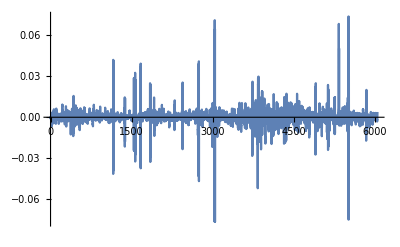

```mathematica
ListLinePlot[rsWethUsdc90dFiltered6Week, PlotRange->All]
```

```mathematica
edistWethUsdc90dFiltered6Week= EstimatedDistribution[rsWethUsdc90dFiltered6Week, StableDistribution[1, aWU90dF6W, bWU90dF6W, locWU90dF6W, scaleWE90dF6W]]
```

StableDistribution[1,1.44156,-0.0954883,-5.04204×10^-6,0.00170617]

```mathematica
rsWethUsdc90dFiltered8Week = Differences[Log[twapsWethUsdc90dFiltered8Week]]
```

{-0.00120673,0.000176452,-0.0000603568,-0.000373722,-0.000389599,0.000559858,-0.00092094,-0.00154871,-0.000905547,-0.000584311,-0.00172231,8041,-0.000801922,0.000895879,0.00162265,0.00187851,0.00260868,0.00351812,0.00180984,0.00092817,0.000511447,-0.000752754,-0.00200428}
 |  |  |  |

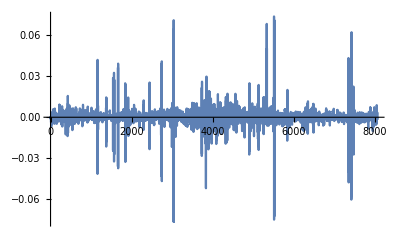

```mathematica
ListLinePlot[rsWethUsdc90dFiltered8Week, PlotRange->All]
```

```mathematica
edistWethUsdc90dFiltered8Week= EstimatedDistribution[rsWethUsdc90dFiltered8Week, StableDistribution[1, aWU90dF8W, bWU90dF8W, locWU90dF8W, scaleWE90dF8W]]
```

StableDistribution[1,1.44755,-0.0635521,-0.0000205867,0.00156225]

```mathematica
(* Not terrible in terms of consistency: particularly on alpha and scale, across different time horizons. Ideally we'd have error estimates here. *)
```

```mathematica
(* Look for stationarity X_t - X_s depends on t-s. So want candles at different time intervals: 10m candles, 30m candles, ... And make sure e.g. scale_30m ^ alpha = 3 * scale_10m ^ alpha *)
```

```mathematica
(* Use the "close" value for "candles" *)
```

```mathematica
(* 10 min candles *)
```

```mathematica
ListLinePlot[twapsWethUsdc90dFiltered, PlotRange->All]
```

-Graphics-

```mathematica
Length[twapsWethUsdc90dFiltered]
```

9139

```mathematica
twapsWethUsdc90dFiltered30MinCandle  = Table[twapsWethUsdc90dFiltered[[i]], {i, 1, Length[twapsWethUsdc90dFiltered], 3}]
```

{2.20799×10^9,2.20558×10^9,2.20513×10^9,2.1977×10^9,2.18452×10^9,2.16595×10^9,2.13229×10^9,2.10155×10^9,2.11006×10^9,2.09959×10^9,2.07922×10^9,2.08201×10^9,2.09635×10^9,2.11173×10^9,2.12707×10^9,2.13829×10^9,2.12948×10^9,2.11405×10^9,2.08876×10^9,2.076×10^9,2.092×10^9,2.12133×10^9,2.14019×10^9,2.14686×10^9,2.15282×10^9,2.17366×10^9,2.18679×10^9,2.18892×10^9,2.18398×10^9,2.1791×10^9,2.19238×10^9,2.21494×10^9,2.20923×10^9,2.1798×10^9,2.16313×10^9,2.18669×10^9,2.2252×10^9,2.25221×10^9,2.2656×10^9,2.28222×10^9,2.28598×10^9,2.29529×10^9,2.31448×10^9,2.31637×10^9,2.31787×10^9,2.33406×10^9,2.33849×10^9,2.32851×10^9,2.327×10^9,2.3323×10^9,2.34079×10^9,2.31713×10^9,2.30593×10^9,2.31671×10^9,2.31917×10^9,2.32558×10^9,2.31566×10^9,2.30019×10^9,2.29969×10^9,2.30422×10^9,2.30039×10^9,2.30631×10^9,2.31432×10^9,2.30176×10^9,2.2911×10^9,2.28608×10^9,2.29267×10^9,2.30062×10^9,2.29931×10^9,2.28086×10^9,2.26585×10^9,2.25879×10^9,2.28924×10^9,2.35018×10^9,2.36951×10^9,2.37608×10^9,2.38804×10^9,2.42281×10^9,2.43288×10^9,2.44261×10^9,2.44522×10^9,2.43264×10^9,2.42349×10^9,2.41978×10^9,2.41306×10^9,2.42622×10^9,2.43004×10^9,2.41259×10^9,2.39108×10^9,2.39224×10^9,2.38836×10^9,2.3728×10^9,2.35824×10^9,2.36015×10^9,2.35909×10^9,2.39834×10^9,2.43401×10^9,2.40246×10^9,2.38868×10^9,2.41463×10^9,2.40558×10^9,2.41017×10^9,2.43149×10^9,2.43943×10^9,2.45836×10^9,2.48092×10^9,2.47252×10^9,2.46728×10^9,2.45963×10^9,2.44154×10^9,2.44538×10^9,2.47271×10^9,2.48836×10^9,2.50627×10^9,2.53708×10^9,2.56074×10^9,2.57431×10^9,2.57025×10^9,2.56804×10^9,2.56592×10^9,2.58211×10^9,2.59214×10^9,2.59943×10^9,2.6257×10^9,2.60893×10^9,2.55281×10^9,2.54473×10^9,2.53653×10^9,2.5154×10^9,2.51323×10^9,2.45851×10^9,2.39405×10^9,2.39695×10^9,2.41739×10^9,2.4136×10^9,2.42198×10^9,2.41881×10^9,2.41421×10^9,2.39325×10^9,2.34364×10^9,2.28152×10^9,2.21876×10^9,2.24012×10^9,2.26274×10^9,2.25792×10^9,2.23095×10^9,2.20518×10^9,2.21536×10^9,2.19372×10^9,2.19679×10^9,2.1814×10^9,2.14905×10^9,2.17754×10^9,2.19521×10^9,2.20198×10^9,2.24864×10^9,2.27401×10^9,2.28763×10^9,2.28949×10^9,2.26861×10^9,2.24668×10^9,2.22708×10^9,2.25694×10^9,2.28157×10^9,2.28855×10^9,2.32178×10^9,2.33238×10^9,2.32483×10^9,2.30586×10^9,2.32069×10^9,2.34455×10^9,2.34906×10^9,2.35986×10^9,2.3539×10^9,2.34445×10^9,2.33339×10^9,2.31699×10^9,2.32377×10^9,2.33811×10^9,2.3484×10^9,2.31129×10^9,2.26549×10^9,2.27699×10^9,2.26117×10^9,2.27259×10^9,2.30558×10^9,2.30824×10^9,2.30738×10^9,2.31167×10^9,2.31036×10^9,2.31729×10^9,2.30616×10^9,2.28115×10^9,2.27517×10^9,2.2841×10^9,2.29036×10^9,2.27321×10^9,2.25823×10^9,2.2328×10^9,2.20809×10^9,2.19895×10^9,2.19647×10^9,2.21535×10^9,2.22751×10^9,2.22182×10^9,2.2085×10^9,2.20086×10^9,2.2091×10^9,2.24249×10^9,2.24966×10^9,2.23852×10^9,2.23331×10^9,2.26192×10^9,2.27821×10^9,2.2762×10^9,2.27331×10^9,2.27615×10^9,2.28907×10^9,2.28902×10^9,2.28126×10^9,2.2637×10^9,2.25289×10^9,2.23579×10^9,2.22636×10^9,2.2202×10^9,2.23311×10^9,2.2419×10^9,2.24391×10^9,2.23764×10^9,2.21278×10^9,2.19271×10^9,2.18846×10^9,2.19508×10^9,2.20061×10^9,2.20039×10^9,2.19265×10^9,2.18244×10^9,2.18744×10^9,2.20087×10^9,2.22071×10^9,2.22228×10^9,2.25415×10^9,2.27257×10^9,2.26725×10^9,2.27791×10^9,2.29906×10^9,2.31112×10^9,2.31573×10^9,2.31413×10^9,2.32147×10^9,2.33998×10^9,2.34487×10^9,2.34076×10^9,2.34246×10^9,2.34044×10^9,2.3292×10^9,2.31663×10^9,2.29961×10^9,2.29939×10^9,2.28655×10^9,2.27635×10^9,2.24366×10^9,2.21107×10^9,2.22275×10^9,2.2594×10^9,2.2803×10^9,2.2981×10^9,2.35786×10^9,2.40696×10^9,2.42174×10^9,2.44476×10^9,2.44403×10^9,2.44623×10^9,2.45112×10^9,2.45812×10^9,2.46427×10^9,2.45375×10^9,2.45302×10^9,2.47045×10^9,2.48101×10^9,2.46507×10^9,2.45548×10^9,2.44595×10^9,2.44154×10^9,2.44323×10^9,2.47179×10^9,2.48714×10^9,2.49573×10^9,2.51503×10^9,2.5143×10^9,2.50391×10^9,2.49414×10^9,2.4989×10^9,2.49147×10^9,2.48799×10^9,2.49484×10^9,2.48933×10^9,2.48286×10^9,2.50791×10^9,2.51417×10^9,2.50156×10^9,2.49477×10^9,2.49079×10^9,2.48389×10^9,2.46433×10^9,2.45422×10^9,2.4924×10^9,2.51584×10^9,2.51696×10^9,2.52155×10^9,2.52264×10^9,2.51238×10^9,2.51242×10^9,2.51481×10^9,2.52143×10^9,2.52365×10^9,2.50823×10^9,2.49751×10^9,2.49901×10^9,2.50984×10^9,2.52488×10^9,2.53955×10^9,2.55421×10^9,2.558×10^9,2.55383×10^9,2.55004×10^9,2.54832×10^9,2.54779×10^9,2.55165×10^9,2.55027×10^9,2.55059×10^9,2.55994×10^9,2.57182×10^9,2.57164×10^9,2.5636×10^9,2.5563×10^9,2.56814×10^9,2.61451×10^9,2.6356×10^9,2.65163×10^9,2.65748×10^9,2.64537×10^9,2.63922×10^9,2.63735×10^9,2.63722×10^9,2.63626×10^9,2.62427×10^9,2.62923×10^9,2.63619×10^9,2.63813×10^9,2.63813×10^9,2.62774×10^9,2.62802×10^9,2.65069×10^9,2.67884×10^9,2.68649×10^9,2.69579×10^9,2.70203×10^9,2.68116×10^9,2.65079×10^9,2.63928×10^9,2.64281×10^9,2.63913×10^9,2.629×10^9,2.6043×10^9,2.58477×10^9,2.5975×10^9,2.61214×10^9,2.61809×10^9,2.61463×10^9,2.6001×10^9,2.60676×10^9,2.62146×10^9,2.64614×10^9,2.68377×10^9,2.70791×10^9,2.71902×10^9,2.70174×10^9,2.69857×10^9,2.71255×10^9,2.70519×10^9,2.68374×10^9,2.68906×10^9,2.7055×10^9,2.71774×10^9,2.71957×10^9,2.72826×10^9,2.72785×10^9,2.83875×10^9,2.72574×10^9,2.71326×10^9,2.71164×10^9,2.73414×10^9,2.74286×10^9,2.72313×10^9,2.72412×10^9,2.73961×10^9,2.74148×10^9,2.72686×10^9,2.71589×10^9,2.71973×10^9,2.72036×10^9,2.71625×10^9,2.70253×10^9,2.68881×10^9,2.68928×10^9,2.69883×10^9,2.71183×10^9,2.72397×10^9,2.72992×10^9,2.73126×10^9,2.72633×10^9,2.71824×10^9,2.73666×10^9,2.7641×10^9,2.76513×10^9,2.76668×10^9,2.76806×10^9,2.76721×10^9,2.78064×10^9,2.78625×10^9,2.77219×10^9,2.76346×10^9,2.7666×10^9,2.77752×10^9,2.78344×10^9,2.76555×10^9,2.74127×10^9,2.73519×10^9,2.72235×10^9,2.71615×10^9,2.72501×10^9,2.72296×10^9,2.71057×10^9,2.70927×10^9,2.71196×10^9,2.73315×10^9,2.7532×10^9,2.76143×10^9,2.76149×10^9,2.75368×10^9,2.74435×10^9,2.73823×10^9,2.74371×10^9,2.74219×10^9,2.74029×10^9,2.74109×10^9,2.74721×10^9,2.75674×10^9,2.76198×10^9,2.76461×10^9,2.77046×10^9,2.78123×10^9,2.78245×10^9,2.77746×10^9,2.77401×10^9,2.78216×10^9,2.78842×10^9,2.76798×10^9,2.77825×10^9,2.76317×10^9,2.75102×10^9,2.74392×10^9,2.74819×10^9,2.74595×10^9,2.74355×10^9,2.75331×10^9,2.7507×10^9,2.7459×10^9,2.74671×10^9,2.75239×10^9,2.76152×10^9,2.76471×10^9,2.76518×10^9,2.76529×10^9,2.77473×10^9,2.77799×10^9,2.77224×10^9,2.7649×10^9,2.75776×10^9,2.75652×10^9,2.75292×10^9,2.7536×10^9,2.76309×10^9,2.77048×10^9,2.76979×10^9,2.76768×10^9,2.79242×10^9,2.82967×10^9,2.83116×10^9,2.83731×10^9,2.84375×10^9,2.84274×10^9,2.85031×10^9,2.86233×10^9,2.85557×10^9,2.85625×10^9,2.85649×10^9,2.85615×10^9,2.8577×10^9,2.83934×10^9,2.83316×10^9,2.83687×10^9,2.83743×10^9,2.84947×10^9,2.8552×10^9,2.86716×10^9,2.87385×10^9,2.86996×10^9,2.86857×10^9,2.86603×10^9,2.85818×10^9,2.85328×10^9,2.86969×10^9,2.88817×10^9,2.90995×10^9,2.92512×10^9,2.93112×10^9,2.93337×10^9,2.92963×10^9,2.92361×10^9,2.93421×10^9,2.93804×10^9,2.92849×10^9,2.93166×10^9,2.93757×10^9,2.94373×10^9,2.94533×10^9,2.93936×10^9,2.93576×10^9,2.93709×10^9,2.94542×10^9,2.95137×10^9,2.94409×10^9,2.91281×10^9,2.91191×10^9,2.91731×10^9,2.91633×10^9,2.91803×10^9,2.90994×10^9,2.89507×10^9,2.88498×10^9,2.87316×10^9,2.87711×10^9,2.88564×10^9,2.90687×10^9,2.91581×10^9,2.91469×10^9,2.9211×10^9,2.92829×10^9,2.92583×10^9,2.92212×10^9,2.9166×10^9,2.91889×10^9,2.81586×10^9,2.92466×10^9,2.93313×10^9,2.93518×10^9,2.93473×10^9,2.938×10^9,2.94487×10^9,2.9592×10^9,2.97281×10^9,2.97352×10^9,2.96885×10^9,2.96959×10^9,2.97396×10^9,2.95729×10^9,2.94192×10^9,2.94644×10^9,2.96718×10^9,2.98637×10^9,2.99205×10^9,3.00858×10^9,3.01749×10^9,3.02486×10^9,3.03939×10^9,3.05285×10^9,3.0537×10^9,3.05571×10^9,3.08027×10^9,3.09292×10^9,3.09069×10^9,3.10229×10^9,3.13349×10^9,3.1563×10^9,3.17874×10^9,3.16874×10^9,3.16742×10^9,3.15435×10^9,3.14946×10^9,3.16539×10^9,3.16459×10^9,3.14581×10^9,3.13545×10^9,3.12068×10^9,3.11962×10^9,3.1519×10^9,3.17054×10^9,3.17194×10^9,3.17997×10^9,3.2328×10^9,3.26847×10^9,3.28874×10^9,3.30984×10^9,3.30975×10^9,3.29632×10^9,3.291×10^9,3.28365×10^9,3.28726×10^9,3.30197×10^9,3.35925×10^9,3.38782×10^9,3.41667×10^9,3.41029×10^9,3.35792×10^9,3.31206×10^9,3.30036×10^9,3.27985×10^9,3.24619×10^9,3.24031×10^9,3.24701×10^9,3.27686×10^9,3.32849×10^9,3.35822×10^9,3.37145×10^9,3.37754×10^9,3.36567×10^9,3.35295×10^9,3.32129×10^9,3.30488×10^9,3.33212×10^9,3.35429×10^9,3.36871×10^9,3.40725×10^9,3.42868×10^9,3.45623×10^9,3.45079×10^9,3.46868×10^9,3.48956×10^9,3.4358×10^9,3.39615×10^9,3.31593×10^9,3.27893×10^9,3.25651×10^9,3.27289×10^9,3.30959×10^9,3.33685×10^9,3.36501×10^9,3.38066×10^9,3.40186×10^9,3.38859×10^9,3.38023×10^9,3.35022×10^9,3.30652×10^9,3.28866×10^9,3.29343×10^9,3.27467×10^9,3.30126×10^9,3.33405×10^9,3.36104×10^9,3.35398×10^9,3.32631×10^9,3.29825×10^9,3.29762×10^9,3.29202×10^9,3.26674×10^9,3.27276×10^9,3.25799×10^9,3.25127×10^9,3.27656×10^9,3.32532×10^9,3.35215×10^9,3.35051×10^9,3.36157×10^9,3.3781×10^9,3.37052×10^9,3.36537×10^9,3.36096×10^9,3.3687×10^9,3.37133×10^9,3.37571×10^9,3.34794×10^9,3.3282×10^9,3.33777×10^9,3.32181×10^9,3.35683×10^9,3.42307×10^9,3.42208×10^9,3.41093×10^9,3.41222×10^9,3.42624×10^9,3.45552×10^9,3.46303×10^9,3.45413×10^9,3.4458×10^9,3.44475×10^9,3.48566×10^9,3.5187×10^9,3.52443×10^9,3.50429×10^9,3.47471×10^9,3.47011×10^9,3.47948×10^9,3.48886×10^9,3.48328×10^9,3.46939×10^9,3.47892×10^9,3.47733×10^9,3.45214×10^9,3.45088×10^9,3.43796×10^9,3.41839×10^9,3.42038×10^9,3.43857×10^9,3.44589×10^9,3.44461×10^9,3.4538×10^9,3.47585×10^9,3.48863×10^9,3.49581×10^9,3.50945×10^9,3.49845×10^9,3.48719×10^9,3.48357×10^9,3.48769×10^9,3.51713×10^9,3.552×10^9,3.57419×10^9,3.5747×10^9,3.57542×10^9,3.56714×10^9,3.506×10^9,3.44775×10^9,3.45856×10^9,3.46594×10^9,3.46529×10^9,3.48588×10^9,3.51189×10^9,3.52508×10^9,3.51816×10^9,3.49862×10^9,3.50526×10^9,3.5073×10^9,3.48685×10^9,3.47043×10^9,3.4508×10^9,3.43222×10^9,3.43042×10^9,3.41047×10^9,3.39232×10^9,3.40425×10^9,3.41145×10^9,3.42648×10^9,3.44033×10^9,3.45443×10^9,3.45358×10^9,3.42884×10^9,3.43182×10^9,3.44556×10^9,3.45631×10^9,3.46416×10^9,3.45656×10^9,3.45334×10^9,3.45006×10^9,3.46291×10^9,3.49336×10^9,3.5041×10^9,3.49927×10^9,3.49464×10^9,3.50865×10^9,3.54307×10^9,3.56177×10^9,3.5549×10^9,3.55588×10^9,3.54119×10^9,3.52548×10^9,3.52329×10^9,3.51894×10^9,3.51978×10^9,3.50502×10^9,3.48574×10^9,3.48605×10^9,3.46672×10^9,3.45079×10^9,3.46729×10^9,3.48421×10^9,3.50477×10^9,3.52755×10^9,3.54106×10^9,3.54076×10^9,3.53457×10^9,3.53249×10^9,3.54604×10^9,3.56992×10^9,3.56091×10^9,3.54756×10^9,3.54105×10^9,3.52933×10^9,3.52497×10^9,3.53244×10^9,3.55503×10^9,3.56615×10^9,3.55476×10^9,3.5612×10^9,3.55885×10^9,3.54436×10^9,3.54639×10^9,3.54691×10^9,3.55441×10^9,3.58262×10^9,3.63149×10^9,3.65586×10^9,3.66661×10^9,3.58062×10^9,3.70349×10^9,3.7727×10^9,3.80744×10^9,3.82237×10^9,3.82697×10^9,3.83128×10^9,3.81804×10^9,3.8228×10^9,3.84762×10^9,3.86521×10^9,3.9009×10^9,3.90859×10^9,3.87884×10^9,3.8787×10^9,3.88709×10^9,3.8657×10^9,3.86859×10^9,3.88178×10^9,3.87545×10^9,3.89524×10^9,3.92358×10^9,3.89336×10^9,3.87154×10^9,3.90608×10^9,3.92121×10^9,3.93227×10^9,3.95786×10^9,3.95864×10^9,3.95018×10^9,3.95068×10^9,3.93913×10^9,3.91603×10^9,3.89265×10^9,3.88966×10^9,3.90861×10^9,3.89569×10^9,3.83389×10^9,3.78543×10^9,3.77862×10^9,3.80714×10^9,3.82276×10^9,3.83344×10^9,3.84046×10^9,3.89274×10^9,3.93896×10^9,3.92455×10^9,3.91396×10^9,3.9148×10^9,3.90568×10^9,3.88842×10^9,3.87271×10^9,3.88696×10^9,3.91011×10^9,3.91573×10^9,3.91105×10^9,3.90068×10^9,3.89418×10^9,3.90845×10^9,3.91273×10^9,3.90923×10^9,3.90809×10^9,3.92922×10^9,3.95091×10^9,3.97542×10^9,4.02269×10^9,4.05106×10^9,4.06387×10^9,4.10581×10^9,4.1096×10^9,4.12089×10^9,4.12402×10^9,4.12081×10^9,4.11287×10^9,4.10294×10^9,4.13228×10^9,4.12322×10^9,4.10555×10^9,4.07891×10^9,4.04088×10^9,4.05166×10^9,4.09337×10^9,4.1261×10^9,4.13685×10^9,4.12469×10^9,4.09416×10^9,4.08194×10^9,4.1178×10^9,4.17201×10^9,4.17438×10^9,4.16758×10^9,4.15324×10^9,4.13623×10^9,4.13164×10^9,4.08348×10^9,3.94978×10^9,3.88932×10^9,3.94076×10^9,4.00082×10^9,3.85186×10^9,3.97904×10^9,3.94583×10^9,3.95799×10^9,3.91788×10^9,3.88678×10^9,3.89697×10^9,3.86068×10^9,3.82168×10^9,3.83452×10^9,3.87339×10^9,3.90141×10^9,3.89215×10^9,3.89406×10^9,3.93413×10^9,3.94848×10^9,3.94697×10^9,3.93445×10^9,3.93244×10^9,3.9596×10^9,4.0189×10^9,4.0512×10^9,4.04583×10^9,3.99749×10^9,3.94772×10^9,3.95243×10^9,3.94069×10^9,3.96281×10^9,3.98022×10^9,4.00156×10^9,4.03681×10^9,4.04201×10^9,4.02386×10^9,4.0344×10^9,4.0643×10^9,4.06711×10^9,4.05645×10^9,4.06441×10^9,4.09817×10^9,4.13384×10^9,4.13162×10^9,4.11788×10^9,4.12715×10^9,4.13899×10^9,4.1597×10^9,4.17178×10^9,4.17413×10^9,4.18279×10^9,4.22934×10^9,4.2641×10^9,4.29803×10^9,4.32243×10^9,4.30775×10^9,4.32228×10^9,4.33479×10^9,4.32988×10^9,4.31475×10^9,4.30912×10^9,4.29292×10^9,4.29344×10^9,4.30192×10^9,4.28969×10^9,4.26228×10^9,4.25303×10^9,4.26471×10^9,4.27796×10^9,4.29802×10^9,4.28761×10^9,4.29269×10^9,4.33239×10^9,4.27056×10^9,4.20803×10^9,4.14873×10^9,4.14267×10^9,4.15545×10^9,4.11796×10^9,4.04037×10^9,4.00064×10^9,4.04288×10^9,4.07428×10^9,4.08557×10^9,4.10879×10^9,4.09757×10^9,4.101×10^9,4.09899×10^9,3.9062×10^9,3.83713×10^9,3.93195×10^9,3.95084×10^9,3.99148×10^9,4.00834×10^9,3.96865×10^9,3.92149×10^9,3.94099×10^9,3.93463×10^9,3.95475×10^9,3.99733×10^9,4.00017×10^9,4.00478×10^9,3.70516×10^9,3.95163×10^9,3.8932×10^9,3.81867×10^9,3.75988×10^9,3.73482×10^9,3.67637×10^9,3.7175×10^9,3.76666×10^9,3.80972×10^9,3.81998×10^9,3.858×10^9,3.87894×10^9,3.83156×10^9,3.79171×10^9,3.81974×10^9,3.74747×10^9,3.64082×10^9,3.66856×10^9,3.64099×10^9,3.63904×10^9,3.67507×10^9,3.6837×10^9,3.71354×10^9,3.74649×10^9,3.74585×10^9,3.73536×10^9,3.69195×10^9,3.66591×10^9,3.74114×10^9,3.79488×10^9,3.84068×10^9,3.86848×10^9,3.84004×10^9,3.8135×10^9,3.80576×10^9,3.80587×10^9,3.80043×10^9,3.79661×10^9,3.81975×10^9,3.84017×10^9,3.82029×10^9,3.84185×10^9,3.87371×10^9,3.88821×10^9,3.91861×10^9,3.95715×10^9,3.96727×10^9,3.96538×10^9,3.99539×10^9,4.01401×10^9,3.99989×10^9,3.98888×10^9,3.99628×10^9,4.03532×10^9,4.05978×10^9,4.1101×10^9,4.14346×10^9,4.13953×10^9,4.12609×10^9,4.12435×10^9,4.11084×10^9,4.08958×10^9,4.07146×10^9,4.06048×10^9,4.03704×10^9,4.00694×10^9,4.02135×10^9,4.04564×10^9,4.07811×10^9,4.08735×10^9,4.09529×10^9,4.08315×10^9,4.05716×10^9,4.08834×10^9,4.10002×10^9,4.08866×10^9,4.06326×10^9,4.04452×10^9,4.04254×10^9,4.02976×10^9,4.01218×10^9,4.01826×10^9,3.99349×10^9,3.94742×10^9,3.92996×10^9,3.91848×10^9,3.92165×10^9,3.90952×10^9,3.87476×10^9,3.84696×10^9,3.86077×10^9,3.88051×10^9,3.89636×10^9,3.91314×10^9,3.90982×10^9,3.88868×10^9,3.8802×10^9,3.89863×10^9,3.87519×10^9,3.8112×10^9,3.75417×10^9,3.75167×10^9,3.7601×10^9,3.75383×10^9,3.71723×10^9,3.72038×10^9,3.77701×10^9,3.80199×10^9,3.80418×10^9,3.80815×10^9,3.78581×10^9,3.72712×10^9,3.68499×10^9,3.74674×10^9,3.78777×10^9,3.82092×10^9,3.82798×10^9,3.82716×10^9,3.81205×10^9,3.80786×10^9,3.82191×10^9,3.81177×10^9,3.79932×10^9,3.82047×10^9,3.86446×10^9,3.85114×10^9,3.83576×10^9,3.81438×10^9,3.80405×10^9,3.81295×10^9,3.82612×10^9,3.83784×10^9,3.83861×10^9,3.81755×10^9,3.79059×10^9,3.74056×10^9,3.709×10^9,3.71543×10^9,3.70714×10^9,3.67614×10^9,3.66337×10^9,3.64593×10^9,3.60695×10^9,3.54398×10^9,3.56603×10^9,3.59328×10^9,3.52941×10^9,3.47452×10^9,3.44514×10^9,3.41747×10^9,3.38722×10^9,3.41376×10^9,3.5025×10^9,3.54028×10^9,3.53978×10^9,3.55881×10^9,3.55339×10^9,3.51549×10^9,3.43759×10^9,3.41854×10^9,3.41376×10^9,3.38051×10^9,3.3191×10^9,3.2503×10^9,3.27644×10^9,3.29619×10^9,3.294×10^9,3.37912×10^9,3.41972×10^9,3.46301×10^9,3.50439×10^9,3.53029×10^9,3.52425×10^9,3.51009×10^9,3.50481×10^9,3.47397×10^9,3.48441×10^9,3.51707×10^9,3.50096×10^9,3.46885×10^9,3.4505×10^9,3.41067×10^9,3.38175×10^9,3.34839×10^9,3.29967×10^9,3.26675×10^9,3.1982×10^9,3.20058×10^9,3.2672×10^9,3.34981×10^9,3.37531×10^9,3.38169×10^9,3.4237×10^9,3.41716×10^9,3.33827×10^9,3.28975×10^9,3.24558×10^9,3.24783×10^9,3.29442×10^9,3.33485×10^9,3.36179×10^9,3.38295×10^9,3.38404×10^9,3.38069×10^9,3.39349×10^9,3.39906×10^9,3.43875×10^9,3.49311×10^9,3.52784×10^9,3.53709×10^9,3.52693×10^9,3.49063×10^9,3.49716×10^9,3.50745×10^9,3.48781×10^9,3.46524×10^9,3.46992×10^9,3.48955×10^9,3.50225×10^9,3.51933×10^9,3.50545×10^9,3.4446×10^9,3.39857×10^9,3.36171×10^9,3.30122×10^9,3.32665×10^9,3.37053×10^9,3.36827×10^9,3.40152×10^9,3.42075×10^9,3.39331×10^9,3.36602×10^9,3.26953×10^9,3.37949×10^9,3.40859×10^9,3.43181×10^9,3.44108×10^9,3.41218×10^9,3.40356×10^9,3.37345×10^9,3.36529×10^9,3.40067×10^9,3.38928×10^9,3.30036×10^9,3.21833×10^9,3.1874×10^9,3.1414×10^9,3.11368×10^9,3.09728×10^9,2.98709×10^9,2.95064×10^9,2.93567×10^9,2.96704×10^9,2.97019×10^9,2.93333×10^9,2.96169×10^9,2.96114×10^9,2.97333×10^9,2.97485×10^9,2.94925×10^9,2.90231×10^9,2.81334×10^9,2.69109×10^9,2.67634×10^9,2.49539×10^9,2.15935×10^9,2.21783×10^9,2.36736×10^9,2.46285×10^9,2.6269×10^9,2.70249×10^9,2.8034×10^9,2.84385×10^9,2.75192×10^9,2.65168×10^9,2.61962×10^9,2.62404×10^9,2.63998×10^9,2.57297×10^9,2.52109×10^9,2.58367×10^9,2.65692×10^9,2.64494×10^9,2.55795×10^9,2.48047×10^9,2.32305×10^9,2.2544×10^9,2.33289×10^9,2.40211×10^9,2.45114×10^9,2.47047×10^9,2.51589×10^9,2.61062×10^9,2.6125×10^9,2.62757×10^9,2.63982×10^9,2.70064×10^9,2.73084×10^9,2.70465×10^9,2.67406×10^9,2.64366×10^9,2.66519×10^9,2.68537×10^9,2.69874×10^9,2.73055×10^9,2.81168×10^9,2.91068×10^9,2.93724×10^9,2.92069×10^9,2.92148×10^9,2.92525×10^9,2.84109×10^9,2.70382×10^9,2.69956×10^9,2.73432×10^9,2.76519×10^9,2.78905×10^9,2.79801×10^9,2.80871×10^9,2.79091×10^9,2.7802×10^9,2.81874×10^9,2.79691×10^9,2.78922×10^9,2.78593×10^9,2.80891×10^9,2.87766×10^9,2.91099×10^9,2.89765×10^9,2.86832×10^9,2.8369×10^9,2.80395×10^9,2.78302×10^9,2.77003×10^9,2.77056×10^9,2.7476×10^9,2.73731×10^9,2.74057×10^9,2.70311×10^9,2.68311×10^9,2.70027×10^9,2.73787×10^9,2.75417×10^9,2.74915×10^9,2.7081×10^9,2.68519×10^9,2.70246×10^9,2.67897×10^9,2.68847×10^9,2.70065×10^9,2.57589×10^9,2.51586×10^9,2.47884×10^9,2.45171×10^9,2.47343×10^9,2.46356×10^9,2.4597×10^9,2.44123×10^9,2.44325×10^9,2.38947×10^9,2.32814×10^9,2.28722×10^9,2.23561×10^9,2.31838×10^9,2.37936×10^9,2.39971×10^9,2.40912×10^9,2.41079×10^9,2.41844×10^9,2.44199×10^9,2.45396×10^9,2.45616×10^9,2.42164×10^9,2.36796×10^9,2.33269×10^9,2.28611×10^9,2.23506×10^9,2.21496×10^9,2.21703×10^9,2.21985×10^9,2.22253×10^9,2.25847×10^9,2.33077×10^9,2.33893×10^9,2.34542×10^9,2.35182×10^9,2.40797×10^9,2.43979×10^9,2.41839×10^9,2.42501×10^9,2.41753×10^9,2.43602×10^9,2.43871×10^9,2.38553×10^9,2.33798×10^9,2.34224×10^9,2.36474×10^9,2.36377×10^9,2.33049×10^9,2.29556×10^9,2.28617×10^9,2.29343×10^9,2.30034×10^9,2.30329×10^9,2.33826×10^9,2.3574×10^9,2.36238×10^9,2.35043×10^9,2.34065×10^9,2.34296×10^9,2.30777×10^9,2.30606×10^9,2.3491×10^9,2.36381×10^9,2.34455×10^9,2.31402×10^9,2.30283×10^9,2.31487×10^9,2.30148×10^9,2.28093×10^9,2.24647×10^9,2.23564×10^9,2.22157×10^9,2.20298×10^9,2.17887×10^9,2.1397×10^9,2.08291×10^9,2.03948×10^9,2.02197×10^9,2.07315×10^9,2.13243×10^9,2.12854×10^9,2.1168×10^9,2.05156×10^9,1.94687×10^9,1.91851×10^9,1.93987×10^9,1.95859×10^9,1.95475×10^9,1.92022×10^9,1.84232×10^9,1.82923×10^9,1.91853×10^9,1.90531×10^9,1.89559×10^9,1.91441×10^9,1.95337×10^9,2.00052×10^9,2.05374×10^9,2.09834×10^9,2.10635×10^9,2.11359×10^9,2.09485×10^9,2.08928×10^9,2.11692×10^9,2.15855×10^9,2.14294×10^9,2.12077×10^9,2.12767×10^9,2.13307×10^9,2.16493×10^9,2.16501×10^9,2.14101×10^9,2.12698×10^9,2.12862×10^9,2.12448×10^9,2.14599×10^9,2.20476×10^9,2.2645×10^9,2.28613×10^9,2.28184×10^9,2.27467×10^9,2.25965×10^9,2.25365×10^9,2.2685×10^9,2.32941×10^9,2.38635×10^9,2.41567×10^9,2.39549×10^9,2.41375×10^9,2.42829×10^9,2.46255×10^9,2.49199×10^9,2.46446×10^9,2.46655×10^9,2.49943×10^9,2.54735×10^9,2.56853×10^9,2.55648×10^9,2.60418×10^9,2.62263×10^9,2.62629×10^9,2.63616×10^9,2.6007×10^9,2.59591×10^9,2.59947×10^9,2.64296×10^9,2.70917×10^9,2.72137×10^9,2.67928×10^9,2.63911×10^9,2.60257×10^9,2.57105×10^9,2.58246×10^9,2.57586×10^9,2.58118×10^9,2.57702×10^9,2.62988×10^9,2.64264×10^9,2.65936×10^9,2.65168×10^9,2.63664×10^9,2.60128×10^9,2.57462×10^9,2.54148×10^9,2.47356×10^9,2.4456×10^9,2.4472×10^9,2.43472×10^9,2.44466×10^9,2.50261×10^9,2.55324×10^9,2.603×10^9,2.6091×10^9,2.59036×10^9,2.58593×10^9,2.58068×10^9,2.57203×10^9,2.57254×10^9,2.59658×10^9,2.58356×10^9,2.55355×10^9,2.54264×10^9,2.55157×10^9,2.57179×10^9,2.62326×10^9,2.6852×10^9,2.70456×10^9,2.69975×10^9,2.6901×10^9,2.68113×10^9,2.71271×10^9,2.76132×10^9,2.80243×10^9,2.80808×10^9,2.82337×10^9,2.81487×10^9,2.80471×10^9,2.81813×10^9,2.81905×10^9,2.85018×10^9,2.87779×10^9,2.87586×10^9,2.8659×10^9,2.85731×10^9,2.85532×10^9,2.83043×10^9,2.80625×10^9,2.8126×10^9,2.83752×10^9,2.85085×10^9,2.80103×10^9,2.74368×10^9,2.75038×10^9,2.74597×10^9,2.73624×10^9,2.75865×10^9,2.72826×10^9,2.69831×10^9,2.71526×10^9,2.73178×10^9,2.73084×10^9,2.72409×10^9,2.74952×10^9,2.79109×10^9,2.79831×10^9,2.80945×10^9,2.82472×10^9,2.83348×10^9,2.8591×10^9,2.85351×10^9,2.80976×10^9,2.76887×10^9,2.72499×10^9,2.7128×10^9,2.68942×10^9,2.67071×10^9,2.67599×10^9,2.68475×10^9,2.68711×10^9,2.70366×10^9,2.72732×10^9,2.74029×10^9,2.74377×10^9,2.73615×10^9,2.75202×10^9,2.77874×10^9,2.78968×10^9,2.79278×10^9,2.79417×10^9,2.80314×10^9,2.81961×10^9,2.81125×10^9,2.81068×10^9,2.83722×10^9,2.84947×10^9,2.85459×10^9,2.82639×10^9,2.80255×10^9,2.78639×10^9,2.77742×10^9,2.78214×10^9,2.78716×10^9,2.78518×10^9,2.77317×10^9,2.75375×10^9,2.75049×10^9,2.73266×10^9,2.74567×10^9,2.77527×10^9,2.77146×10^9,2.75624×10^9,2.74038×10^9,2.72327×10^9,2.71845×10^9,2.69812×10^9,2.71233×10^9,2.72264×10^9,2.72305×10^9,2.71735×10^9,2.7036×10^9,2.67653×10^9,2.6655×10^9,2.62059×10^9,2.5572×10^9,2.55426×10^9,2.5644×10^9,2.56129×10^9,2.54249×10^9,2.48811×10^9,2.47769×10^9,2.49588×10^9,2.50258×10^9,2.48381×10^9,2.47901×10^9,2.53097×10^9,2.57723×10^9,2.59247×10^9,2.57588×10^9,2.55763×10^9,2.55849×10^9,2.54233×10^9,2.50841×10^9,2.49725×10^9,2.49658×10^9,2.49829×10^9,2.52018×10^9,2.51674×10^9,2.50578×10^9,2.47639×10^9,2.39925×10^9,2.36618×10^9,2.37814×10^9,2.38693×10^9,2.40845×10^9,2.43233×10^9,2.46615×10^9,2.5117×10^9,2.52485×10^9,2.51506×10^9,2.51065×10^9,2.52151×10^9,2.52258×10^9,2.51232×10^9,2.51491×10^9,2.54846×10^9,2.54896×10^9,2.53907×10^9,2.5197×10^9,2.49615×10^9,2.47453×10^9,2.44633×10^9,2.42609×10^9,2.429×10^9,2.42782×10^9,2.422×10^9,2.43445×10^9,2.4289×10^9,2.40055×10^9,2.37344×10^9,2.38376×10^9,2.38374×10^9,2.34077×10^9,2.31907×10^9,2.32936×10^9,2.346×10^9,2.31097×10^9,2.27229×10^9,2.26726×10^9,2.25483×10^9,2.24699×10^9,2.23587×10^9,2.23923×10^9,2.25227×10^9,2.26551×10^9,2.26669×10^9,2.2745×10^9,2.28777×10^9,2.2424×10^9,2.21746×10^9,2.21857×10^9,2.22336×10^9,2.25095×10^9,2.2787×10^9,2.28735×10^9,2.28894×10^9,2.29923×10^9,2.32744×10^9,2.36767×10^9,2.39486×10^9,2.4183×10^9,2.43264×10^9,2.4441×10^9,2.44064×10^9,2.43304×10^9,2.42846×10^9,2.41804×10^9,2.41287×10^9,2.41231×10^9,2.42129×10^9,2.43547×10^9,2.4069×10^9,2.38932×10^9,2.38832×10^9,2.3693×10^9,2.35911×10^9,2.36411×10^9,2.38198×10^9,2.40372×10^9,2.41598×10^9,2.4291×10^9,2.44192×10^9,2.45625×10^9,2.45334×10^9,2.4448×10^9,2.44309×10^9,2.43691×10^9,2.43316×10^9,2.42175×10^9,2.40453×10^9,2.39364×10^9,2.38925×10^9,2.37053×10^9,2.34751×10^9,2.31865×10^9,2.3045×10^9,2.3066×10^9,2.30512×10^9,2.30474×10^9,2.3022×10^9,2.30704×10^9,2.32221×10^9,2.33568×10^9,2.36074×10^9,2.40452×10^9,2.58176×10^9,2.72165×10^9,2.69345×10^9,2.65542×10^9,2.63788×10^9,2.65041×10^9,2.63788×10^9,2.63922×10^9,2.65214×10^9,2.67845×10^9,2.68763×10^9,2.66311×10^9,2.65425×10^9,2.63816×10^9,2.59494×10^9,2.57622×10^9,2.57384×10^9,2.58182×10^9,2.60018×10^9,2.61311×10^9,2.61164×10^9,2.58529×10^9,2.56346×10^9,2.59909×10^9,2.6244×10^9,2.60015×10^9,2.57192×10^9,2.56446×10^9,2.56409×10^9,2.54941×10^9,2.54594×10^9,2.55961×10^9,2.56788×10^9,2.55841×10^9,2.54766×10^9,2.55881×10^9,2.57164×10^9,2.56499×10^9,2.59317×10^9,2.59253×10^9,2.60102×10^9,2.62693×10^9,2.61326×10^9,2.58536×10^9,2.56877×10^9,2.58754×10^9,2.60571×10^9,2.61927×10^9,2.62338×10^9,2.62736×10^9,2.62887×10^9,2.6224×10^9,2.63193×10^9,2.64179×10^9,2.64567×10^9,2.70085×10^9,2.69064×10^9,2.69117×10^9,2.69869×10^9,2.6943×10^9,2.69063×10^9,2.49924×10^9,2.68315×10^9,2.69689×10^9,2.70558×10^9,2.70218×10^9,2.72211×10^9,2.73595×10^9,2.7537×10^9,2.7772×10^9,2.78665×10^9,2.77823×10^9,2.76457×10^9,2.76037×10^9,2.76474×10^9,2.76456×10^9,2.76428×10^9,2.75976×10^9,2.75045×10^9,2.72843×10^9,2.72586×10^9,2.72082×10^9,2.70339×10^9,2.69879×10^9,2.71108×10^9,2.7039×10^9,2.702×10^9,2.70198×10^9,2.68777×10^9,2.69129×10^9,2.70814×10^9,2.72735×10^9,2.75585×10^9,2.78288×10^9,2.8057×10^9,2.82306×10^9,2.8356×10^9,2.82496×10^9,2.82846×10^9,2.83791×10^9,2.8477×10^9,2.87147×10^9,2.88601×10^9,2.86477×10^9,2.83304×10^9,2.81076×10^9,2.82326×10^9,2.82161×10^9,2.79364×10^9,2.78443×10^9,2.79149×10^9,2.7987×10^9,2.79408×10^9,2.81341×10^9,2.83155×10^9,2.83497×10^9,2.82645×10^9,2.80887×10^9,2.7951×10^9,2.79509×10^9,2.80006×10^9,2.81496×10^9,2.82871×10^9,2.82611×10^9,2.83574×10^9,2.85037×10^9,2.85143×10^9,2.82282×10^9,2.79018×10^9,2.74063×10^9,2.72433×10^9,2.7311×10^9,2.74829×10^9,2.75951×10^9,2.74784×10^9,2.71862×10^9,2.67608×10^9,2.66176×10^9,2.63275×10^9,2.61836×10^9,2.62653×10^9,2.63181×10^9,2.62981×10^9,2.64083×10^9,2.65079×10^9,2.64138×10^9,2.63591×10^9,2.60966×10^9,2.6007×10^9,2.64316×10^9,2.65359×10^9,2.63716×10^9,2.63505×10^9,2.64703×10^9,2.65819×10^9,2.67026×10^9,2.66823×10^9,2.69048×10^9,2.69806×10^9,2.69511×10^9,2.70081×10^9,2.69148×10^9,2.68905×10^9,2.70154×10^9,2.7213×10^9,2.72686×10^9,2.72595×10^9,2.71131×10^9,2.68776×10^9,2.70267×10^9,2.74104×10^9,2.76195×10^9,2.76586×10^9,2.76524×10^9,2.76066×10^9,2.76643×10^9,2.76729×10^9,2.77163×10^9,2.77716×10^9,2.77477×10^9,2.77033×10^9,2.77631×10^9,2.78586×10^9,2.79759×10^9,2.79361×10^9,2.80212×10^9,2.79215×10^9,2.73449×10^9,2.71228×10^9,2.69948×10^9,2.65956×10^9,2.63962×10^9,2.63983×10^9,2.63459×10^9,2.62623×10^9,2.61744×10^9,2.60797×10^9,2.62608×10^9,2.64143×10^9,2.63127×10^9,2.62719×10^9,2.62616×10^9,2.62747×10^9,2.62989×10^9,2.62485×10^9,2.62214×10^9,2.62734×10^9,2.60023×10^9,2.57013×10^9,2.57834×10^9,2.58446×10^9,2.59993×10^9,2.62131×10^9,2.62991×10^9,2.64994×10^9,2.67156×10^9,2.68378×10^9,2.68251×10^9,2.67543×10^9,2.67719×10^9,2.6817×10^9,2.68139×10^9,2.68312×10^9,2.67978×10^9,2.66487×10^9,2.67241×10^9,2.69257×10^9,2.71018×10^9,2.72531×10^9,2.73032×10^9,2.72154×10^9,2.71266×10^9,2.70823×10^9,2.70398×10^9,2.70237×10^9,2.69055×10^9,2.67172×10^9,2.66929×10^9,2.69476×10^9,2.71782×10^9,2.7227×10^9,2.72622×10^9,2.71799×10^9,2.70194×10^9,2.69153×10^9,2.68853×10^9,2.685×10^9,2.68051×10^9,2.68329×10^9,2.69713×10^9,2.70694×10^9,2.69792×10^9,2.6891×10^9,2.69724×10^9,2.71029×10^9,2.7386×10^9,2.75564×10^9,2.76588×10^9,2.78674×10^9,2.79236×10^9,2.79008×10^9,2.77705×10^9,2.77828×10^9,2.77712×10^9,2.7764×10^9,2.78011×10^9,2.77746×10^9,2.75973×10^9,2.75832×10^9,2.76084×10^9,2.75931×10^9,2.77055×10^9,2.7938×10^9,2.8225×10^9,2.82688×10^9,2.81911×10^9,2.81454×10^9,2.82858×10^9,2.82294×10^9,2.79691×10^9,2.77959×10^9,2.77393×10^9,2.77829×10^9,2.7767×10^9,2.76748×10^9,2.74457×10^9,2.72537×10^9,2.70967×10^9,2.69883×10^9,2.70253×10^9,2.71989×10^9,2.70689×10^9,2.64823×10^9,2.60727×10^9,2.61717×10^9,2.62121×10^9,2.61386×10^9,2.59933×10^9,2.59071×10^9,2.58776×10^9,2.60328×10^9,2.60115×10^9,2.56237×10^9,2.49122×10^9,2.47989×10^9,2.50517×10^9,2.50604×10^9,2.49126×10^9,2.48745×10^9,2.49184×10^9,2.48588×10^9,2.50335×10^9,2.52579×10^9,2.54051×10^9,2.518×10^9,2.5028×10^9,2.50364×10^9,2.49588×10^9,2.50658×10^9,2.53617×10^9,2.52012×10^9,2.49993×10^9,2.47676×10^9,2.42425×10^9,2.38443×10^9,2.3518×10^9,2.37037×10^9,2.40567×10^9,2.40551×10^9,2.40453×10^9,2.42494×10^9,2.45774×10^9,2.47183×10^9,2.48481×10^9,2.50014×10^9,2.52481×10^9,2.52815×10^9,2.52444×10^9,2.49916×10^9,2.5288×10^9,2.52309×10^9,2.4992×10^9,2.47285×10^9,2.4625×10^9,2.44919×10^9,2.43519×10^9,2.44831×10^9,2.45876×10^9,2.44405×10^9,2.43392×10^9,2.46379×10^9,2.48103×10^9,2.49834×10^9,2.52738×10^9,2.52692×10^9,2.5083×10^9,2.49402×10^9,2.4921×10^9,2.49398×10^9,2.49461×10^9,2.50451×10^9,2.50947×10^9,2.54774×10^9,2.55559×10^9,2.5386×10^9,2.53209×10^9,2.52718×10^9,2.51659×10^9,2.55263×10^9,2.57317×10^9,2.59411×10^9,2.60497×10^9,2.59312×10^9,2.58688×10^9,2.5722×10^9,2.56606×10^9,2.56383×10^9,2.56608×10^9,2.57223×10^9,2.59279×10^9,2.621×10^9,2.60234×10^9,2.5748×10^9,2.59489×10^9,2.58697×10^9,2.5926×10^9,2.58242×10^9,2.57037×10^9,2.57687×10^9,2.58071×10^9,2.56923×10^9,2.5561×10^9,2.54331×10^9,2.5329×10^9,2.53427×10^9,2.54006×10^9,2.54461×10^9,2.5441×10^9,2.53271×10^9,2.51581×10^9,2.53727×10^9,2.58194×10^9,2.59084×10^9,2.57865×10^9,2.56632×10^9,2.55376×10^9,2.5499×10^9,2.54316×10^9,2.53541×10^9,2.52307×10^9,2.51913×10^9,2.50866×10^9,2.49173×10^9,2.47936×10^9,2.46765×10^9,2.46821×10^9,2.4673×10^9,2.46478×10^9,2.46221×10^9,2.44645×10^9,2.44993×10^9,2.46705×10^9,2.47741×10^9,2.48608×10^9,2.49042×10^9,2.48324×10^9,2.47243×10^9,2.44513×10^9,2.42047×10^9,2.41871×10^9,2.41968×10^9,2.44352×10^9,2.46017×10^9,2.46358×10^9,2.47198×10^9,2.47808×10^9,2.47164×10^9,2.45501×10^9,2.4363×10^9,2.43454×10^9,2.44903×10^9,2.45652×10^9,2.45647×10^9,2.46398×10^9,2.4689×10^9,2.47405×10^9,2.47141×10^9,2.46458×10^9,2.45833×10^9,2.46239×10^9,2.46981×10^9,2.4674×10^9,2.45503×10^9,2.43153×10^9,2.41865×10^9,2.39778×10^9,2.38369×10^9,2.39666×10^9,2.39855×10^9,2.40051×10^9,2.40891×10^9,2.40405×10^9,2.39932×10^9,2.38351×10^9,2.35237×10^9,2.35353×10^9,2.36311×10^9,2.34577×10^9,2.34386×10^9,2.34265×10^9,2.33974×10^9,2.31954×10^9,2.2892×10^9,2.27621×10^9,2.28625×10^9,2.29259×10^9,2.29496×10^9,2.28681×10^9,2.28863×10^9,2.29041×10^9,2.29229×10^9,2.30512×10^9,2.316×10^9,2.31623×10^9,2.31452×10^9,2.31736×10^9,2.32021×10^9,2.35447×10^9,2.38545×10^9,2.38303×10^9,2.40632×10^9,2.43428×10^9,2.4379×10^9,2.43069×10^9,2.41939×10^9,2.42076×10^9,2.40946×10^9,2.39804×10^9,2.39009×10^9,2.39102×10^9,2.39183×10^9,2.40315×10^9,2.41322×10^9,2.4156×10^9,2.41925×10^9,2.41723×10^9,2.41511×10^9,2.41086×10^9,2.40498×10^9,2.40033×10^9,2.38659×10^9,2.38226×10^9,2.37984×10^9,2.36533×10^9,2.38012×10^9,2.40374×10^9,2.40643×10^9,2.4031×10^9,2.3825×10^9,2.3474×10^9,2.33556×10^9,2.33823×10^9,2.33131×10^9,2.32342×10^9,2.32081×10^9,2.32866×10^9,2.33704×10^9,2.33264×10^9,2.3432×10^9,2.35439×10^9,2.35424×10^9,2.3622×10^9,2.36876×10^9,2.37014×10^9,2.36812×10^9,2.37018×10^9,2.3621×10^9,2.35654×10^9,2.35666×10^9,2.34627×10^9,2.34085×10^9,2.34225×10^9,2.36042×10^9,2.39059×10^9,2.40002×10^9,2.41272×10^9,2.43132×10^9,2.43884×10^9,2.43456×10^9,2.44854×10^9,2.48487×10^9,2.51404×10^9,2.53103×10^9,2.52591×10^9,2.5118×10^9,2.50664×10^9,2.50272×10^9,2.49909×10^9,2.50074×10^9,2.50431×10^9,2.50303×10^9,2.50029×10^9,2.49041×10^9,2.47665×10^9,2.48077×10^9,2.48417×10^9,2.49405×10^9,2.50055×10^9,2.49807×10^9,2.49988×10^9,2.49903×10^9,2.48864×10^9,2.48209×10^9,2.48086×10^9,2.47645×10^9,2.47964×10^9,2.48929×10^9,2.48611×10^9,2.48178×10^9,2.48645×10^9,2.51605×10^9,2.54793×10^9,2.56483×10^9,2.56762×10^9,2.55813×10^9,2.57003×10^9,2.58343×10^9,2.5725×10^9,2.57265×10^9,2.57212×10^9,2.556×10^9,2.53308×10^9,2.53355×10^9,2.53643×10^9,2.54689×10^9,2.5611×10^9,2.56273×10^9,2.56353×10^9,2.5649×10^9,2.57333×10^9,2.59201×10^9,2.60762×10^9,2.59752×10^9,2.58387×10^9,2.58238×10^9,2.5902×10^9,2.59209×10^9,2.59378×10^9,2.61267×10^9,2.62592×10^9,2.62044×10^9,2.62374×10^9,2.62023×10^9,2.61138×10^9,2.61314×10^9,2.6094×10^9,2.58468×10^9,2.58329×10^9,2.5865×10^9,2.58406×10^9,2.58218×10^9,2.57982×10^9,2.58794×10^9,2.59278×10^9,2.59359×10^9,2.58436×10^9,2.56016×10^9,2.54683×10^9,2.54289×10^9,2.5465×10^9,2.55399×10^9,2.55972×10^9,2.58105×10^9,2.59808×10^9,2.57857×10^9,2.54913×10^9,2.52793×10^9,2.52679×10^9,2.52737×10^9,2.53009×10^9,2.54115×10^9,2.55399×10^9,2.55497×10^9,2.53779×10^9,2.52682×10^9,2.51656×10^9,2.51529×10^9,2.52228×10^9,2.52524×10^9,2.52178×10^9,2.519×10^9,2.52078×10^9,2.52753×10^9,2.52965×10^9,2.52804×10^9,2.5276×10^9,2.53589×10^9,2.54479×10^9,2.53898×10^9,2.5324×10^9,2.52605×10^9,2.52058×10^9,2.51265×10^9,2.48981×10^9,2.46614×10^9,2.45519×10^9,2.44939×10^9,2.45367×10^9,2.45691×10^9,2.45047×10^9,2.43198×10^9,2.41822×10^9,2.42762×10^9,2.31109×10^9,2.40256×10^9,2.41333×10^9,2.41042×10^9,2.41865×10^9,2.42319×10^9,2.41268×10^9,2.40385×10^9,2.40414×10^9,2.40619×10^9,2.3962×10^9,2.37018×10^9,2.36452×10^9,2.3838×10^9,2.39556×10^9,2.40298×10^9,2.41157×10^9,2.42034×10^9,2.42747×10^9,2.43219×10^9,2.42955×10^9,2.42291×10^9,2.4217×10^9,2.43031×10^9,2.44407×10^9,2.45061×10^9,2.4474×10^9,2.44121×10^9,2.43615×10^9,2.4392×10^9,2.44177×10^9,2.43837×10^9,2.43259×10^9,2.40859×10^9,2.39074×10^9,2.38315×10^9,2.37916×10^9,2.39098×10^9,2.39871×10^9,2.40467×10^9,2.39666×10^9,2.3143×10^9,2.33631×10^9,2.31908×10^9,2.32223×10^9,2.34206×10^9,2.33709×10^9,2.34155×10^9,2.34329×10^9,2.34057×10^9,2.34057×10^9,2.34173×10^9,2.35436×10^9,2.36907×10^9,2.36956×10^9,2.36636×10^9,2.3527×10^9,2.33696×10^9,2.32799×10^9,2.33461×10^9,2.33904×10^9,2.34276×10^9,2.34836×10^9,2.35613×10^9,2.35375×10^9,2.34112×10^9,2.3329×10^9,2.33401×10^9,2.34251×10^9,2.3487×10^9,2.34806×10^9,2.32989×10^9,2.30489×10^9,2.31022×10^9,2.32648×10^9,2.32244×10^9,2.30585×10^9,2.289×10^9,2.27901×10^9,2.27041×10^9,2.25559×10^9,2.24882×10^9,2.24034×10^9,2.22348×10^9,2.22774×10^9,2.22957×10^9,2.21619×10^9,2.19688×10^9,2.16659×10^9,2.15795×10^9,2.16355×10^9,2.18433×10^9,2.19464×10^9,2.20334×10^9,2.21074×10^9,2.20867×10^9,2.20876×10^9,2.22131×10^9,2.23624×10^9,2.24424×10^9,2.24613×10^9,2.24788×10^9,2.23751×10^9,2.21647×10^9,2.19507×10^9,2.18767×10^9,2.19684×10^9,2.20943×10^9,2.22987×10^9,2.23837×10^9,2.23671×10^9,2.23071×10^9,2.23602×10^9,2.24349×10^9,2.24976×10^9,2.24318×10^9,2.23191×10^9,2.22888×10^9,2.23067×10^9,2.23657×10^9,2.25462×10^9,2.24555×10^9,2.2331×10^9,2.23207×10^9,2.23867×10^9,2.24877×10^9,2.24583×10^9,2.24105×10^9,2.23886×10^9,2.23722×10^9,2.22718×10^9,2.20648×10^9,2.19979×10^9,2.20945×10^9,2.21834×10^9,2.21682×10^9,2.21943×10^9,2.22236×10^9,2.20584×10^9,2.18729×10^9,2.1815×10^9,2.17645×10^9,2.16199×10^9,2.16053×10^9,2.17492×10^9,2.17999×10^9,2.17149×10^9,2.17245×10^9,2.18257×10^9,2.18765×10^9,2.20031×10^9,2.20896×10^9,2.21112×10^9,2.21032×10^9,2.20704×10^9,2.20257×10^9,2.19768×10^9,2.1968×10^9,2.18635×10^9,2.17951×10^9,2.16475×10^9,2.11701×10^9,2.09601×10^9,2.08351×10^9,2.06717×10^9,2.06409×10^9,2.08467×10^9,2.08603×10^9,2.08772×10^9,2.10111×10^9,2.11543×10^9,2.1176×10^9,2.12279×10^9,2.12632×10^9,2.13156×10^9,2.13533×10^9,2.14895×10^9,2.17697×10^9,2.2148×10^9,2.24219×10^9,2.25121×10^9,2.25775×10^9,2.26022×10^9,2.25307×10^9,2.24877×10^9,2.24413×10^9,2.23587×10^9,2.22902×10^9,2.22441×10^9,2.21159×10^9,2.20166×10^9,2.18567×10^9,2.17594×10^9,2.14525×10^9,2.10239×10^9,2.1013×10^9,2.10912×10^9,2.11309×10^9,2.05386×10^9,2.01959×10^9,2.00998×10^9,2.01738×10^9,2.01795×10^9,2.00542×10^9,2.00406×10^9,1.97741×10^9,1.94033×10^9,1.93946×10^9,1.96084×10^9,1.95532×10^9,1.94806×10^9,1.97879×10^9,1.99652×10^9,1.99989×10^9,1.98739×10^9,1.97141×10^9,1.93911×10^9,1.93346×10^9,1.92986×10^9,1.93422×10^9,1.94715×10^9,1.93646×10^9,1.94017×10^9,1.94139×10^9,1.92696×10^9,1.90045×10^9,1.88846×10^9,1.88578×10^9,1.90211×10^9,1.88782×10^9,1.8904×10^9,1.93414×10^9,1.95379×10^9,1.94882×10^9,1.95217×10^9,1.96786×10^9,1.97426×10^9,1.96598×10^9,1.96436×10^9,1.94725×10^9,1.93824×10^9,1.94286×10^9,1.94357×10^9,1.93818×10^9,1.90442×10^9,1.88158×10^9,1.87313×10^9,1.86881×10^9,1.88642×10^9,1.88938×10^9,1.86925×10^9,1.84003×10^9,1.79496×10^9,1.77392×10^9,1.73802×10^9,1.75722×10^9,1.82214×10^9,1.86773×10^9,1.89728×10^9,1.90119×10^9,1.90336×10^9,1.90558×10^9,1.9238×10^9,1.92154×10^9,1.90547×10^9,1.91232×10^9,1.92273×10^9,1.9017×10^9,1.88144×10^9,1.8817×10^9,1.87469×10^9,1.86401×10^9,1.87015×10^9,1.9301×10^9,1.975×10^9,1.99613×10^9,2.0091×10^9,2.00821×10^9,2.00938×10^9,2.00966×10^9,2.00501×10^9,2.01228×10^9,2.02694×10^9,2.0198×10^9,2.00953×10^9,2.00925×10^9,2.00144×10^9,1.98795×10^9,1.99305×10^9,1.99395×10^9,2.00323×10^9,2.00126×10^9,1.99606×10^9,2.00207×10^9,2.01758×10^9,2.01308×10^9,1.99587×10^9,1.99268×10^9,1.98233×10^9,1.98434×10^9,1.99112×10^9,1.98614×10^9,1.97779×10^9,1.96233×10^9,1.95545×10^9,1.95016×10^9,1.93358×10^9,1.93201×10^9,1.93936×10^9,1.94099×10^9,1.94363×10^9,1.94727×10^9,1.94986×10^9,1.96307×10^9,1.96588×10^9,1.94737×10^9,1.92875×10^9,1.91134×10^9,1.89777×10^9,1.89904×10^9,1.90516×10^9,1.90495×10^9,1.90457×10^9,1.91042×10^9,1.92016×10^9,1.92311×10^9,1.92701×10^9,1.9312×10^9,1.92814×10^9,1.93136×10^9,1.94227×10^9,1.94566×10^9,1.94327×10^9,1.93889×10^9,1.94263×10^9,1.96344×10^9,1.97518×10^9,1.96996×10^9,1.96587×10^9,1.96583×10^9,1.9704×10^9,1.99017×10^9,1.99819×10^9,1.99063×10^9,2.01084×10^9,2.02226×10^9,2.02254×10^9,2.02107×10^9,2.0188×10^9,2.01498×10^9,2.00995×10^9,2.00581×10^9,2.00207×10^9,1.99754×10^9,1.98927×10^9,1.98314×10^9,1.98647×10^9,1.99599×10^9,2.00116×10^9,1.98101×10^9,1.97596×10^9,1.99995×10^9,2.00941×10^9,1.9972×10^9,1.99248×10^9,1.987×10^9,1.97906×10^9,1.97119×10^9,1.96543×10^9,1.96337×10^9,1.95394×10^9,1.93851×10^9,1.9311×10^9,1.93112×10^9,1.93244×10^9,1.91373×10^9,1.89449×10^9,1.87577×10^9,1.86088×10^9,1.86221×10^9,1.86056×10^9,1.8507×10^9,1.8558×10^9,1.85596×10^9,1.82466×10^9,1.82019×10^9,1.82473×10^9,1.81559×10^9,1.82125×10^9,1.81803×10^9,1.82968×10^9,1.84157×10^9,1.85241×10^9,1.85048×10^9,1.85751×10^9,1.8543×10^9,1.8509×10^9,1.8411×10^9,1.81792×10^9,1.81562×10^9,1.81654×10^9,1.82381×10^9,1.82338×10^9,1.81441×10^9,1.82072×10^9,1.82119×10^9,1.82877×10^9,1.8378×10^9,1.8353×10^9,1.83007×10^9,1.80237×10^9,1.76562×10^9,1.7415×10^9,1.73026×10^9,1.73457×10^9,1.75722×10^9,1.76333×10^9,1.7683×10^9,1.78986×10^9,1.79735×10^9,1.79888×10^9,1.79042×10^9,1.76258×10^9,1.74571×10^9,1.76782×10^9,1.77325×10^9,1.7657×10^9,1.75189×10^9,1.75637×10^9,1.76299×10^9,1.78093×10^9,1.78696×10^9,1.78759×10^9,1.78372×10^9,1.7707×10^9,1.76361×10^9,1.76165×10^9,1.76902×10^9,1.77759×10^9,1.78698×10^9,1.79765×10^9,1.82361×10^9,1.83502×10^9,1.84322×10^9,1.86132×10^9,1.87626×10^9,1.87954×10^9,1.8849×10^9,1.88006×10^9,1.87166×10^9,1.86223×10^9,1.86045×10^9,1.86469×10^9,1.86664×10^9,1.85953×10^9,1.83946×10^9,1.82664×10^9,1.8232×10^9,1.82588×10^9,1.83581×10^9,1.84602×10^9,1.85408×10^9,1.85149×10^9,1.83965×10^9,1.83347×10^9,1.83623×10^9,1.83947×10^9,1.84144×10^9,1.83555×10^9,1.8269×10^9,1.82249×10^9,1.81643×10^9,1.81597×10^9,1.8156×10^9,1.8203×10^9,1.82396×10^9,1.82167×10^9,1.82609×10^9,1.88163×10^9,1.94104×10^9,1.95155×10^9,1.96693×10^9,1.97995×10^9,1.98443×10^9,1.97518×10^9,1.96833×10^9,1.97334×10^9,1.97487×10^9,1.97217×10^9,1.97318×10^9,1.97088×10^9,1.97432×10^9,1.97681×10^9,2.01868×10^9,1.98876×10^9,2.01748×10^9,2.04771×10^9,2.05892×10^9,2.05925×10^9,2.05052×10^9,2.0229×10^9,1.99984×10^9,1.99659×10^9,1.99921×10^9,2.00719×10^9,2.01164×10^9,2.01368×10^9,2.01745×10^9,2.04033×10^9,2.07186×10^9,2.10458×10^9,2.11057×10^9,2.10625×10^9,2.0951×10^9,2.08438×10^9,2.08704×10^9,2.10781×10^9,2.12203×10^9,2.1201×10^9,2.12913×10^9,2.12609×10^9,2.10716×10^9,2.09126×10^9,2.08046×10^9,2.08246×10^9,2.10566×10^9,2.12692×10^9,2.12367×10^9,2.12054×10^9,2.10785×10^9,2.09813×10^9,2.10564×10^9,2.11572×10^9,2.1202×10^9,2.1124×10^9,2.11002×10^9,2.13072×10^9,2.15734×10^9,2.15163×10^9,2.13095×10^9,2.13778×10^9,2.14671×10^9,2.15615×10^9,2.15845×10^9,2.17026×10^9,2.18068×10^9,2.17893×10^9,2.17741×10^9,2.18451×10^9,2.20963×10^9,2.22444×10^9,2.22374×10^9,2.22446×10^9,2.21686×10^9,2.2179×10^9,2.22613×10^9,2.23271×10^9,2.22795×10^9,2.21872×10^9,2.2187×10^9,2.21876×10^9,2.22029×10^9,2.20271×10^9,2.19923×10^9,2.19742×10^9,2.18074×10^9,2.17518×10^9,2.16655×10^9,2.16459×10^9,2.17271×10^9,2.16208×10^9,2.16103×10^9,2.1663×10^9,2.15493×10^9,2.13349×10^9,2.12823×10^9,2.11211×10^9,2.10606×10^9,2.12026×10^9,2.13541×10^9,2.13823×10^9,2.1508×10^9,2.15859×10^9,2.14254×10^9,2.12394×10^9,2.12244×10^9,2.12801×10^9,2.13745×10^9,2.14671×10^9,2.15469×10^9,2.14654×10^9,2.13319×10^9,2.13626×10^9,2.13479×10^9,2.11587×10^9,2.10415×10^9}

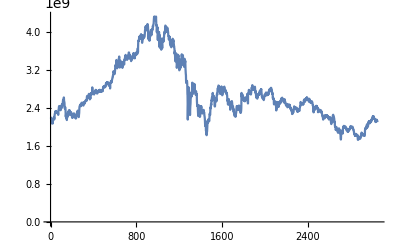

```mathematica
ListLinePlot[twapsWethUsdc90dFiltered30MinCandle]
```

```mathematica
Length[twapsWethUsdc90dFiltered30MinCandle]
```

3047

```mathematica
twapsWethUsdc90dFiltered1HourCandle = Table[twapsWethUsdc90dFiltered[[i]], {i, 1, Length[twapsWethUsdc90dFiltered], 6}]
```

{2.20799×10^9,2.20513×10^9,2.18452×10^9,2.13229×10^9,2.11006×10^9,2.07922×10^9,2.09635×10^9,2.12707×10^9,2.12948×10^9,2.08876×10^9,2.092×10^9,2.14019×10^9,2.15282×10^9,2.18679×10^9,2.18398×10^9,2.19238×10^9,2.20923×10^9,2.16313×10^9,2.2252×10^9,2.2656×10^9,2.28598×10^9,2.31448×10^9,2.31787×10^9,2.33849×10^9,2.327×10^9,2.34079×10^9,2.30593×10^9,2.31917×10^9,2.31566×10^9,2.29969×10^9,2.30039×10^9,2.31432×10^9,2.2911×10^9,2.29267×10^9,2.29931×10^9,2.26585×10^9,2.28924×10^9,2.36951×10^9,2.38804×10^9,2.43288×10^9,2.44522×10^9,2.42349×10^9,2.41306×10^9,2.43004×10^9,2.39108×10^9,2.38836×10^9,2.35824×10^9,2.35909×10^9,2.43401×10^9,2.38868×10^9,2.40558×10^9,2.43149×10^9,2.45836×10^9,2.47252×10^9,2.45963×10^9,2.44538×10^9,2.48836×10^9,2.53708×10^9,2.57431×10^9,2.56804×10^9,2.58211×10^9,2.59943×10^9,2.60893×10^9,2.54473×10^9,2.5154×10^9,2.45851×10^9,2.39695×10^9,2.4136×10^9,2.41881×10^9,2.39325×10^9,2.28152×10^9,2.24012×10^9,2.25792×10^9,2.20518×10^9,2.19372×10^9,2.1814×10^9,2.17754×10^9,2.20198×10^9,2.27401×10^9,2.28949×10^9,2.24668×10^9,2.25694×10^9,2.28855×10^9,2.33238×10^9,2.30586×10^9,2.34455×10^9,2.35986×10^9,2.34445×10^9,2.31699×10^9,2.33811×10^9,2.31129×10^9,2.27699×10^9,2.27259×10^9,2.30824×10^9,2.31167×10^9,2.31729×10^9,2.28115×10^9,2.2841×10^9,2.27321×10^9,2.2328×10^9,2.19895×10^9,2.21535×10^9,2.22182×10^9,2.20086×10^9,2.24249×10^9,2.23852×10^9,2.26192×10^9,2.2762×10^9,2.27615×10^9,2.28902×10^9,2.2637×10^9,2.23579×10^9,2.2202×10^9,2.2419×10^9,2.23764×10^9,2.19271×10^9,2.19508×10^9,2.20039×10^9,2.18244×10^9,2.20087×10^9,2.22228×10^9,2.27257×10^9,2.27791×10^9,2.31112×10^9,2.31413×10^9,2.33998×10^9,2.34076×10^9,2.34044×10^9,2.31663×10^9,2.29939×10^9,2.27635×10^9,2.21107×10^9,2.2594×10^9,2.2981×10^9,2.40696×10^9,2.44476×10^9,2.44623×10^9,2.45812×10^9,2.45375×10^9,2.47045×10^9,2.46507×10^9,2.44595×10^9,2.44323×10^9,2.48714×10^9,2.51503×10^9,2.50391×10^9,2.4989×10^9,2.48799×10^9,2.48933×10^9,2.50791×10^9,2.50156×10^9,2.49079×10^9,2.46433×10^9,2.4924×10^9,2.51696×10^9,2.52264×10^9,2.51242×10^9,2.52143×10^9,2.50823×10^9,2.49901×10^9,2.52488×10^9,2.55421×10^9,2.55383×10^9,2.54832×10^9,2.55165×10^9,2.55059×10^9,2.57182×10^9,2.5636×10^9,2.56814×10^9,2.6356×10^9,2.65748×10^9,2.63922×10^9,2.63722×10^9,2.62427×10^9,2.63619×10^9,2.63813×10^9,2.62802×10^9,2.67884×10^9,2.69579×10^9,2.68116×10^9,2.63928×10^9,2.63913×10^9,2.6043×10^9,2.5975×10^9,2.61809×10^9,2.6001×10^9,2.62146×10^9,2.68377×10^9,2.71902×10^9,2.69857×10^9,2.70519×10^9,2.68906×10^9,2.71774×10^9,2.72826×10^9,2.83875×10^9,2.71326×10^9,2.73414×10^9,2.72313×10^9,2.73961×10^9,2.72686×10^9,2.71973×10^9,2.71625×10^9,2.68881×10^9,2.69883×10^9,2.72397×10^9,2.73126×10^9,2.71824×10^9,2.7641×10^9,2.76668×10^9,2.76721×10^9,2.78625×10^9,2.76346×10^9,2.77752×10^9,2.76555×10^9,2.73519×10^9,2.71615×10^9,2.72296×10^9,2.70927×10^9,2.73315×10^9,2.76143×10^9,2.75368×10^9,2.73823×10^9,2.74219×10^9,2.74109×10^9,2.75674×10^9,2.76461×10^9,2.78123×10^9,2.77746×10^9,2.78216×10^9,2.76798×10^9,2.76317×10^9,2.74392×10^9,2.74595×10^9,2.75331×10^9,2.7459×10^9,2.75239×10^9,2.76471×10^9,2.76529×10^9,2.77799×10^9,2.7649×10^9,2.75652×10^9,2.7536×10^9,2.77048×10^9,2.76768×10^9,2.82967×10^9,2.83731×10^9,2.84274×10^9,2.86233×10^9,2.85625×10^9,2.85615×10^9,2.83934×10^9,2.83687×10^9,2.84947×10^9,2.86716×10^9,2.86996×10^9,2.86603×10^9,2.85328×10^9,2.88817×10^9,2.92512×10^9,2.93337×10^9,2.92361×10^9,2.93804×10^9,2.93166×10^9,2.94373×10^9,2.93936×10^9,2.93709×10^9,2.95137×10^9,2.91281×10^9,2.91731×10^9,2.91803×10^9,2.89507×10^9,2.87316×10^9,2.88564×10^9,2.91581×10^9,2.9211×10^9,2.92583×10^9,2.9166×10^9,2.81586×10^9,2.93313×10^9,2.93473×10^9,2.94487×10^9,2.97281×10^9,2.96885×10^9,2.97396×10^9,2.94192×10^9,2.96718×10^9,2.99205×10^9,3.01749×10^9,3.03939×10^9,3.0537×10^9,3.08027×10^9,3.09069×10^9,3.13349×10^9,3.17874×10^9,3.16742×10^9,3.14946×10^9,3.16459×10^9,3.13545×10^9,3.11962×10^9,3.17054×10^9,3.17997×10^9,3.26847×10^9,3.30984×10^9,3.29632×10^9,3.28365×10^9,3.30197×10^9,3.38782×10^9,3.41029×10^9,3.31206×10^9,3.27985×10^9,3.24031×10^9,3.27686×10^9,3.35822×10^9,3.37754×10^9,3.35295×10^9,3.30488×10^9,3.35429×10^9,3.40725×10^9,3.45623×10^9,3.46868×10^9,3.4358×10^9,3.31593×10^9,3.25651×10^9,3.30959×10^9,3.36501×10^9,3.40186×10^9,3.38023×10^9,3.30652×10^9,3.29343×10^9,3.30126×10^9,3.36104×10^9,3.32631×10^9,3.29762×10^9,3.26674×10^9,3.25799×10^9,3.27656×10^9,3.35215×10^9,3.36157×10^9,3.37052×10^9,3.36096×10^9,3.37133×10^9,3.34794×10^9,3.33777×10^9,3.35683×10^9,3.42208×10^9,3.41222×10^9,3.45552×10^9,3.45413×10^9,3.44475×10^9,3.5187×10^9,3.50429×10^9,3.47011×10^9,3.48886×10^9,3.46939×10^9,3.47733×10^9,3.45088×10^9,3.41839×10^9,3.43857×10^9,3.44461×10^9,3.47585×10^9,3.49581×10^9,3.49845×10^9,3.48357×10^9,3.51713×10^9,3.57419×10^9,3.57542×10^9,3.506×10^9,3.45856×10^9,3.46529×10^9,3.51189×10^9,3.51816×10^9,3.50526×10^9,3.48685×10^9,3.4508×10^9,3.43042×10^9,3.39232×10^9,3.41145×10^9,3.44033×10^9,3.45358×10^9,3.43182×10^9,3.45631×10^9,3.45656×10^9,3.45006×10^9,3.49336×10^9,3.49927×10^9,3.50865×10^9,3.56177×10^9,3.55588×10^9,3.52548×10^9,3.51894×10^9,3.50502×10^9,3.48605×10^9,3.45079×10^9,3.48421×10^9,3.52755×10^9,3.54076×10^9,3.53249×10^9,3.56992×10^9,3.54756×10^9,3.52933×10^9,3.53244×10^9,3.56615×10^9,3.5612×10^9,3.54436×10^9,3.54691×10^9,3.58262×10^9,3.65586×10^9,3.58062×10^9,3.7727×10^9,3.82237×10^9,3.83128×10^9,3.8228×10^9,3.86521×10^9,3.90859×10^9,3.8787×10^9,3.8657×10^9,3.88178×10^9,3.89524×10^9,3.89336×10^9,3.90608×10^9,3.93227×10^9,3.95864×10^9,3.95068×10^9,3.91603×10^9,3.88966×10^9,3.89569×10^9,3.78543×10^9,3.80714×10^9,3.83344×10^9,3.89274×10^9,3.92455×10^9,3.9148×10^9,3.88842×10^9,3.88696×10^9,3.91573×10^9,3.90068×10^9,3.90845×10^9,3.90923×10^9,3.92922×10^9,3.97542×10^9,4.05106×10^9,4.10581×10^9,4.12089×10^9,4.12081×10^9,4.10294×10^9,4.12322×10^9,4.07891×10^9,4.05166×10^9,4.1261×10^9,4.12469×10^9,4.08194×10^9,4.17201×10^9,4.16758×10^9,4.13623×10^9,4.08348×10^9,3.88932×10^9,4.00082×10^9,3.97904×10^9,3.95799×10^9,3.88678×10^9,3.86068×10^9,3.83452×10^9,3.90141×10^9,3.89406×10^9,3.94848×10^9,3.93445×10^9,3.9596×10^9,4.0512×10^9,3.99749×10^9,3.95243×10^9,3.96281×10^9,4.00156×10^9,4.04201×10^9,4.0344×10^9,4.06711×10^9,4.06441×10^9,4.13384×10^9,4.11788×10^9,4.13899×10^9,4.17178×10^9,4.18279×10^9,4.2641×10^9,4.32243×10^9,4.32228×10^9,4.32988×10^9,4.30912×10^9,4.29344×10^9,4.28969×10^9,4.25303×10^9,4.27796×10^9,4.28761×10^9,4.33239×10^9,4.20803×10^9,4.14267×10^9,4.11796×10^9,4.00064×10^9,4.07428×10^9,4.10879×10^9,4.101×10^9,3.9062×10^9,3.93195×10^9,3.99148×10^9,3.96865×10^9,3.94099×10^9,3.95475×10^9,4.00017×10^9,3.70516×10^9,3.8932×10^9,3.75988×10^9,3.67637×10^9,3.76666×10^9,3.81998×10^9,3.87894×10^9,3.79171×10^9,3.74747×10^9,3.66856×10^9,3.63904×10^9,3.6837×10^9,3.74649×10^9,3.73536×10^9,3.66591×10^9,3.79488×10^9,3.86848×10^9,3.8135×10^9,3.80587×10^9,3.79661×10^9,3.84017×10^9,3.84185×10^9,3.88821×10^9,3.95715×10^9,3.96538×10^9,4.01401×10^9,3.98888×10^9,4.03532×10^9,4.1101×10^9,4.13953×10^9,4.12435×10^9,4.08958×10^9,4.06048×10^9,4.00694×10^9,4.04564×10^9,4.08735×10^9,4.08315×10^9,4.08834×10^9,4.08866×10^9,4.04452×10^9,4.02976×10^9,4.01826×10^9,3.94742×10^9,3.91848×10^9,3.90952×10^9,3.84696×10^9,3.88051×10^9,3.91314×10^9,3.88868×10^9,3.89863×10^9,3.8112×10^9,3.75167×10^9,3.75383×10^9,3.72038×10^9,3.80199×10^9,3.80815×10^9,3.72712×10^9,3.74674×10^9,3.82092×10^9,3.82716×10^9,3.80786×10^9,3.81177×10^9,3.82047×10^9,3.85114×10^9,3.81438×10^9,3.81295×10^9,3.83784×10^9,3.81755×10^9,3.74056×10^9,3.71543×10^9,3.67614×10^9,3.64593×10^9,3.54398×10^9,3.59328×10^9,3.47452×10^9,3.41747×10^9,3.41376×10^9,3.54028×10^9,3.55881×10^9,3.51549×10^9,3.41854×10^9,3.38051×10^9,3.2503×10^9,3.29619×10^9,3.37912×10^9,3.46301×10^9,3.53029×10^9,3.51009×10^9,3.47397×10^9,3.51707×10^9,3.46885×10^9,3.41067×10^9,3.34839×10^9,3.26675×10^9,3.20058×10^9,3.34981×10^9,3.38169×10^9,3.41716×10^9,3.28975×10^9,3.24783×10^9,3.33485×10^9,3.38295×10^9,3.38069×10^9,3.39906×10^9,3.49311×10^9,3.53709×10^9,3.49063×10^9,3.50745×10^9,3.46524×10^9,3.48955×10^9,3.51933×10^9,3.4446×10^9,3.36171×10^9,3.32665×10^9,3.36827×10^9,3.42075×10^9,3.36602×10^9,3.37949×10^9,3.43181×10^9,3.41218×10^9,3.37345×10^9,3.40067×10^9,3.30036×10^9,3.1874×10^9,3.11368×10^9,2.98709×10^9,2.93567×10^9,2.97019×10^9,2.96169×10^9,2.97333×10^9,2.94925×10^9,2.81334×10^9,2.67634×10^9,2.15935×10^9,2.36736×10^9,2.6269×10^9,2.8034×10^9,2.75192×10^9,2.61962×10^9,2.63998×10^9,2.52109×10^9,2.65692×10^9,2.55795×10^9,2.32305×10^9,2.33289×10^9,2.45114×10^9,2.51589×10^9,2.6125×10^9,2.63982×10^9,2.73084×10^9,2.67406×10^9,2.66519×10^9,2.69874×10^9,2.81168×10^9,2.93724×10^9,2.92148×10^9,2.84109×10^9,2.69956×10^9,2.76519×10^9,2.79801×10^9,2.79091×10^9,2.81874×10^9,2.78922×10^9,2.80891×10^9,2.91099×10^9,2.86832×10^9,2.80395×10^9,2.77003×10^9,2.7476×10^9,2.74057×10^9,2.68311×10^9,2.73787×10^9,2.74915×10^9,2.68519×10^9,2.67897×10^9,2.70065×10^9,2.51586×10^9,2.45171×10^9,2.46356×10^9,2.44123×10^9,2.38947×10^9,2.28722×10^9,2.31838×10^9,2.39971×10^9,2.41079×10^9,2.44199×10^9,2.45616×10^9,2.36796×10^9,2.28611×10^9,2.21496×10^9,2.21985×10^9,2.25847×10^9,2.33893×10^9,2.35182×10^9,2.43979×10^9,2.42501×10^9,2.43602×10^9,2.38553×10^9,2.34224×10^9,2.36377×10^9,2.29556×10^9,2.29343×10^9,2.30329×10^9,2.3574×10^9,2.35043×10^9,2.34296×10^9,2.30606×10^9,2.36381×10^9,2.31402×10^9,2.31487×10^9,2.28093×10^9,2.23564×10^9,2.20298×10^9,2.1397×10^9,2.03948×10^9,2.07315×10^9,2.12854×10^9,2.05156×10^9,1.91851×10^9,1.95859×10^9,1.92022×10^9,1.82923×10^9,1.90531×10^9,1.91441×10^9,2.00052×10^9,2.09834×10^9,2.11359×10^9,2.08928×10^9,2.15855×10^9,2.12077×10^9,2.13307×10^9,2.16501×10^9,2.12698×10^9,2.12448×10^9,2.20476×10^9,2.28613×10^9,2.27467×10^9,2.25365×10^9,2.32941×10^9,2.41567×10^9,2.41375×10^9,2.46255×10^9,2.46446×10^9,2.49943×10^9,2.56853×10^9,2.60418×10^9,2.62629×10^9,2.6007×10^9,2.59947×10^9,2.70917×10^9,2.67928×10^9,2.60257×10^9,2.58246×10^9,2.58118×10^9,2.62988×10^9,2.65936×10^9,2.63664×10^9,2.57462×10^9,2.47356×10^9,2.4472×10^9,2.44466×10^9,2.55324×10^9,2.6091×10^9,2.58593×10^9,2.57203×10^9,2.59658×10^9,2.55355×10^9,2.55157×10^9,2.62326×10^9,2.70456×10^9,2.6901×10^9,2.71271×10^9,2.80243×10^9,2.82337×10^9,2.80471×10^9,2.81905×10^9,2.87779×10^9,2.8659×10^9,2.85532×10^9,2.80625×10^9,2.83752×10^9,2.80103×10^9,2.75038×10^9,2.73624×10^9,2.72826×10^9,2.71526×10^9,2.73084×10^9,2.74952×10^9,2.79831×10^9,2.82472×10^9,2.8591×10^9,2.80976×10^9,2.72499×10^9,2.68942×10^9,2.67599×10^9,2.68711×10^9,2.72732×10^9,2.74377×10^9,2.75202×10^9,2.78968×10^9,2.79417×10^9,2.81961×10^9,2.81068×10^9,2.84947×10^9,2.82639×10^9,2.78639×10^9,2.78214×10^9,2.78518×10^9,2.75375×10^9,2.73266×10^9,2.77527×10^9,2.75624×10^9,2.72327×10^9,2.69812×10^9,2.72264×10^9,2.71735×10^9,2.67653×10^9,2.62059×10^9,2.55426×10^9,2.56129×10^9,2.48811×10^9,2.49588×10^9,2.48381×10^9,2.53097×10^9,2.59247×10^9,2.55763×10^9,2.54233×10^9,2.49725×10^9,2.49829×10^9,2.51674×10^9,2.47639×10^9,2.36618×10^9,2.38693×10^9,2.43233×10^9,2.5117×10^9,2.51506×10^9,2.52151×10^9,2.51232×10^9,2.54846×10^9,2.53907×10^9,2.49615×10^9,2.44633×10^9,2.429×10^9,2.422×10^9,2.4289×10^9,2.37344×10^9,2.38374×10^9,2.31907×10^9,2.346×10^9,2.27229×10^9,2.25483×10^9,2.23587×10^9,2.25227×10^9,2.26669×10^9,2.28777×10^9,2.21746×10^9,2.22336×10^9,2.2787×10^9,2.28894×10^9,2.32744×10^9,2.39486×10^9,2.43264×10^9,2.44064×10^9,2.42846×10^9,2.41287×10^9,2.42129×10^9,2.4069×10^9,2.38832×10^9,2.35911×10^9,2.38198×10^9,2.41598×10^9,2.44192×10^9,2.45334×10^9,2.44309×10^9,2.43316×10^9,2.40453×10^9,2.38925×10^9,2.34751×10^9,2.3045×10^9,2.30512×10^9,2.3022×10^9,2.32221×10^9,2.36074×10^9,2.58176×10^9,2.69345×10^9,2.63788×10^9,2.63788×10^9,2.65214×10^9,2.68763×10^9,2.65425×10^9,2.59494×10^9,2.57384×10^9,2.60018×10^9,2.61164×10^9,2.56346×10^9,2.6244×10^9,2.57192×10^9,2.56409×10^9,2.54594×10^9,2.56788×10^9,2.54766×10^9,2.57164×10^9,2.59317×10^9,2.60102×10^9,2.61326×10^9,2.56877×10^9,2.60571×10^9,2.62338×10^9,2.62887×10^9,2.63193×10^9,2.64567×10^9,2.69064×10^9,2.69869×10^9,2.69063×10^9,2.68315×10^9,2.70558×10^9,2.72211×10^9,2.7537×10^9,2.78665×10^9,2.76457×10^9,2.76474×10^9,2.76428×10^9,2.75045×10^9,2.72586×10^9,2.70339×10^9,2.71108×10^9,2.702×10^9,2.68777×10^9,2.70814×10^9,2.75585×10^9,2.8057×10^9,2.8356×10^9,2.82846×10^9,2.8477×10^9,2.88601×10^9,2.83304×10^9,2.82326×10^9,2.79364×10^9,2.79149×10^9,2.79408×10^9,2.83155×10^9,2.82645×10^9,2.7951×10^9,2.80006×10^9,2.82871×10^9,2.83574×10^9,2.85143×10^9,2.79018×10^9,2.72433×10^9,2.74829×10^9,2.74784×10^9,2.67608×10^9,2.63275×10^9,2.62653×10^9,2.62981×10^9,2.65079×10^9,2.63591×10^9,2.6007×10^9,2.65359×10^9,2.63505×10^9,2.65819×10^9,2.66823×10^9,2.69806×10^9,2.70081×10^9,2.68905×10^9,2.7213×10^9,2.72595×10^9,2.68776×10^9,2.74104×10^9,2.76586×10^9,2.76066×10^9,2.76729×10^9,2.77716×10^9,2.77033×10^9,2.78586×10^9,2.79361×10^9,2.79215×10^9,2.71228×10^9,2.65956×10^9,2.63983×10^9,2.62623×10^9,2.60797×10^9,2.64143×10^9,2.62719×10^9,2.62747×10^9,2.62485×10^9,2.62734×10^9,2.57013×10^9,2.58446×10^9,2.62131×10^9,2.64994×10^9,2.68378×10^9,2.67543×10^9,2.6817×10^9,2.68312×10^9,2.66487×10^9,2.69257×10^9,2.72531×10^9,2.72154×10^9,2.70823×10^9,2.70237×10^9,2.67172×10^9,2.69476×10^9,2.7227×10^9,2.71799×10^9,2.69153×10^9,2.685×10^9,2.68329×10^9,2.70694×10^9,2.6891×10^9,2.71029×10^9,2.75564×10^9,2.78674×10^9,2.79008×10^9,2.77828×10^9,2.7764×10^9,2.77746×10^9,2.75832×10^9,2.75931×10^9,2.7938×10^9,2.82688×10^9,2.81454×10^9,2.82294×10^9,2.77959×10^9,2.77829×10^9,2.76748×10^9,2.72537×10^9,2.69883×10^9,2.71989×10^9,2.64823×10^9,2.61717×10^9,2.61386×10^9,2.59071×10^9,2.60328×10^9,2.56237×10^9,2.47989×10^9,2.50604×10^9,2.48745×10^9,2.48588×10^9,2.52579×10^9,2.518×10^9,2.50364×10^9,2.50658×10^9,2.52012×10^9,2.47676×10^9,2.38443×10^9,2.37037×10^9,2.40551×10^9,2.42494×10^9,2.47183×10^9,2.50014×10^9,2.52815×10^9,2.49916×10^9,2.52309×10^9,2.47285×10^9,2.44919×10^9,2.44831×10^9,2.44405×10^9,2.46379×10^9,2.49834×10^9,2.52692×10^9,2.49402×10^9,2.49398×10^9,2.50451×10^9,2.54774×10^9,2.5386×10^9,2.52718×10^9,2.55263×10^9,2.59411×10^9,2.59312×10^9,2.5722×10^9,2.56383×10^9,2.57223×10^9,2.621×10^9,2.5748×10^9,2.58697×10^9,2.58242×10^9,2.57687×10^9,2.56923×10^9,2.54331×10^9,2.53427×10^9,2.54461×10^9,2.53271×10^9,2.53727×10^9,2.59084×10^9,2.56632×10^9,2.5499×10^9,2.53541×10^9,2.51913×10^9,2.49173×10^9,2.46765×10^9,2.4673×10^9,2.46221×10^9,2.44993×10^9,2.47741×10^9,2.49042×10^9,2.47243×10^9,2.42047×10^9,2.41968×10^9,2.46017×10^9,2.47198×10^9,2.47164×10^9,2.4363×10^9,2.44903×10^9,2.45647×10^9,2.4689×10^9,2.47141×10^9,2.45833×10^9,2.46981×10^9,2.45503×10^9,2.41865×10^9,2.38369×10^9,2.39855×10^9,2.40891×10^9,2.39932×10^9,2.35237×10^9,2.36311×10^9,2.34386×10^9,2.33974×10^9,2.2892×10^9,2.28625×10^9,2.29496×10^9,2.28863×10^9,2.29229×10^9,2.316×10^9,2.31452×10^9,2.32021×10^9,2.38545×10^9,2.40632×10^9,2.4379×10^9,2.41939×10^9,2.40946×10^9,2.39009×10^9,2.39183×10^9,2.41322×10^9,2.41925×10^9,2.41511×10^9,2.40498×10^9,2.38659×10^9,2.37984×10^9,2.38012×10^9,2.40643×10^9,2.3825×10^9,2.33556×10^9,2.33131×10^9,2.32081×10^9,2.33704×10^9,2.3432×10^9,2.35424×10^9,2.36876×10^9,2.36812×10^9,2.3621×10^9,2.35666×10^9,2.34085×10^9,2.36042×10^9,2.40002×10^9,2.43132×10^9,2.43456×10^9,2.48487×10^9,2.53103×10^9,2.5118×10^9,2.50272×10^9,2.50074×10^9,2.50303×10^9,2.49041×10^9,2.48077×10^9,2.49405×10^9,2.49807×10^9,2.49903×10^9,2.48209×10^9,2.47645×10^9,2.48929×10^9,2.48178×10^9,2.51605×10^9,2.56483×10^9,2.55813×10^9,2.58343×10^9,2.57265×10^9,2.556×10^9,2.53355×10^9,2.54689×10^9,2.56273×10^9,2.5649×10^9,2.59201×10^9,2.59752×10^9,2.58238×10^9,2.59209×10^9,2.61267×10^9,2.62044×10^9,2.62023×10^9,2.61314×10^9,2.58468×10^9,2.5865×10^9,2.58218×10^9,2.58794×10^9,2.59359×10^9,2.56016×10^9,2.54289×10^9,2.55399×10^9,2.58105×10^9,2.57857×10^9,2.52793×10^9,2.52737×10^9,2.54115×10^9,2.55497×10^9,2.52682×10^9,2.51529×10^9,2.52524×10^9,2.519×10^9,2.52753×10^9,2.52804×10^9,2.53589×10^9,2.53898×10^9,2.52605×10^9,2.51265×10^9,2.46614×10^9,2.44939×10^9,2.45691×10^9,2.43198×10^9,2.42762×10^9,2.40256×10^9,2.41042×10^9,2.42319×10^9,2.40385×10^9,2.40619×10^9,2.37018×10^9,2.3838×10^9,2.40298×10^9,2.42034×10^9,2.43219×10^9,2.42291×10^9,2.43031×10^9,2.45061×10^9,2.44121×10^9,2.4392×10^9,2.43837×10^9,2.40859×10^9,2.38315×10^9,2.39098×10^9,2.40467×10^9,2.3143×10^9,2.31908×10^9,2.34206×10^9,2.34155×10^9,2.34057×10^9,2.34173×10^9,2.36907×10^9,2.36636×10^9,2.33696×10^9,2.33461×10^9,2.34276×10^9,2.35613×10^9,2.34112×10^9,2.33401×10^9,2.3487×10^9,2.32989×10^9,2.31022×10^9,2.32244×10^9,2.289×10^9,2.27041×10^9,2.24882×10^9,2.22348×10^9,2.22957×10^9,2.19688×10^9,2.15795×10^9,2.18433×10^9,2.20334×10^9,2.20867×10^9,2.22131×10^9,2.24424×10^9,2.24788×10^9,2.21647×10^9,2.18767×10^9,2.20943×10^9,2.23837×10^9,2.23071×10^9,2.24349×10^9,2.24318×10^9,2.22888×10^9,2.23657×10^9,2.24555×10^9,2.23207×10^9,2.24877×10^9,2.24105×10^9,2.23722×10^9,2.20648×10^9,2.20945×10^9,2.21682×10^9,2.22236×10^9,2.18729×10^9,2.17645×10^9,2.16053×10^9,2.17999×10^9,2.17245×10^9,2.18765×10^9,2.20896×10^9,2.21032×10^9,2.20257×10^9,2.1968×10^9,2.17951×10^9,2.11701×10^9,2.08351×10^9,2.06409×10^9,2.08603×10^9,2.10111×10^9,2.1176×10^9,2.12632×10^9,2.13533×10^9,2.17697×10^9,2.24219×10^9,2.25775×10^9,2.25307×10^9,2.24413×10^9,2.22902×10^9,2.21159×10^9,2.18567×10^9,2.14525×10^9,2.1013×10^9,2.11309×10^9,2.01959×10^9,2.01738×10^9,2.00542×10^9,1.97741×10^9,1.93946×10^9,1.95532×10^9,1.97879×10^9,1.99989×10^9,1.97141×10^9,1.93346×10^9,1.93422×10^9,1.93646×10^9,1.94139×10^9,1.90045×10^9,1.88578×10^9,1.88782×10^9,1.93414×10^9,1.94882×10^9,1.96786×10^9,1.96598×10^9,1.94725×10^9,1.94286×10^9,1.93818×10^9,1.88158×10^9,1.86881×10^9,1.88938×10^9,1.84003×10^9,1.77392×10^9,1.75722×10^9,1.86773×10^9,1.90119×10^9,1.90558×10^9,1.92154×10^9,1.91232×10^9,1.9017×10^9,1.8817×10^9,1.86401×10^9,1.9301×10^9,1.99613×10^9,2.00821×10^9,2.00966×10^9,2.01228×10^9,2.0198×10^9,2.00925×10^9,1.98795×10^9,1.99395×10^9,2.00126×10^9,2.00207×10^9,2.01308×10^9,1.99268×10^9,1.98434×10^9,1.98614×10^9,1.96233×10^9,1.95016×10^9,1.93201×10^9,1.94099×10^9,1.94727×10^9,1.96307×10^9,1.94737×10^9,1.91134×10^9,1.89904×10^9,1.90495×10^9,1.91042×10^9,1.92311×10^9,1.9312×10^9,1.93136×10^9,1.94566×10^9,1.93889×10^9,1.96344×10^9,1.96996×10^9,1.96583×10^9,1.99017×10^9,1.99063×10^9,2.02226×10^9,2.02107×10^9,2.01498×10^9,2.00581×10^9,1.99754×10^9,1.98314×10^9,1.99599×10^9,1.98101×10^9,1.99995×10^9,1.9972×10^9,1.987×10^9,1.97119×10^9,1.96337×10^9,1.93851×10^9,1.93112×10^9,1.91373×10^9,1.87577×10^9,1.86221×10^9,1.8507×10^9,1.85596×10^9,1.82019×10^9,1.81559×10^9,1.81803×10^9,1.84157×10^9,1.85048×10^9,1.8543×10^9,1.8411×10^9,1.81562×10^9,1.82381×10^9,1.81441×10^9,1.82119×10^9,1.8378×10^9,1.83007×10^9,1.76562×10^9,1.73026×10^9,1.75722×10^9,1.7683×10^9,1.79735×10^9,1.79042×10^9,1.74571×10^9,1.77325×10^9,1.75189×10^9,1.76299×10^9,1.78696×10^9,1.78372×10^9,1.76361×10^9,1.76902×10^9,1.78698×10^9,1.82361×10^9,1.84322×10^9,1.87626×10^9,1.8849×10^9,1.87166×10^9,1.86045×10^9,1.86664×10^9,1.83946×10^9,1.8232×10^9,1.83581×10^9,1.85408×10^9,1.83965×10^9,1.83623×10^9,1.84144×10^9,1.8269×10^9,1.81643×10^9,1.8156×10^9,1.82396×10^9,1.82609×10^9,1.94104×10^9,1.96693×10^9,1.98443×10^9,1.96833×10^9,1.97487×10^9,1.97318×10^9,1.97432×10^9,2.01868×10^9,2.01748×10^9,2.05892×10^9,2.05052×10^9,1.99984×10^9,1.99921×10^9,2.01164×10^9,2.01745×10^9,2.07186×10^9,2.11057×10^9,2.0951×10^9,2.08704×10^9,2.12203×10^9,2.12913×10^9,2.10716×10^9,2.08046×10^9,2.10566×10^9,2.12367×10^9,2.10785×10^9,2.10564×10^9,2.1202×10^9,2.11002×10^9,2.15734×10^9,2.13095×10^9,2.14671×10^9,2.15845×10^9,2.18068×10^9,2.17741×10^9,2.20963×10^9,2.22374×10^9,2.21686×10^9,2.22613×10^9,2.22795×10^9,2.2187×10^9,2.22029×10^9,2.19923×10^9,2.18074×10^9,2.16655×10^9,2.17271×10^9,2.16103×10^9,2.15493×10^9,2.12823×10^9,2.10606×10^9,2.13541×10^9,2.1508×10^9,2.14254×10^9,2.12244×10^9,2.13745×10^9,2.15469×10^9,2.13319×10^9,2.13479×10^9,2.10415×10^9}

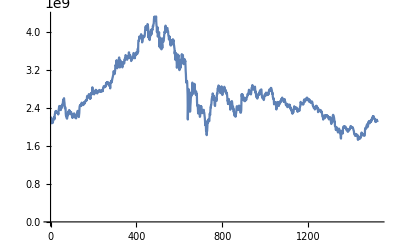

```mathematica
ListLinePlot[twapsWethUsdc90dFiltered1HourCandle]
```

```mathematica
Length[twapsWethUsdc90dFiltered1HourCandle]
```

1524

```mathematica
twapsWethUsdc90dFiltered2HourCandle = Table[twapsWethUsdc90dFiltered[[i]], {i, 1, Length[twapsWethUsdc90dFiltered], 12}]
```

{2.20799×10^9,2.18452×10^9,2.11006×10^9,2.09635×10^9,2.12948×10^9,2.092×10^9,2.15282×10^9,2.18398×10^9,2.20923×10^9,2.2252×10^9,2.28598×10^9,2.31787×10^9,2.327×10^9,2.30593×10^9,2.31566×10^9,2.30039×10^9,2.2911×10^9,2.29931×10^9,2.28924×10^9,2.38804×10^9,2.44522×10^9,2.41306×10^9,2.39108×10^9,2.35824×10^9,2.43401×10^9,2.40558×10^9,2.45836×10^9,2.45963×10^9,2.48836×10^9,2.57431×10^9,2.58211×10^9,2.60893×10^9,2.5154×10^9,2.39695×10^9,2.41881×10^9,2.28152×10^9,2.25792×10^9,2.19372×10^9,2.17754×10^9,2.27401×10^9,2.24668×10^9,2.28855×10^9,2.30586×10^9,2.35986×10^9,2.31699×10^9,2.31129×10^9,2.27259×10^9,2.31167×10^9,2.28115×10^9,2.27321×10^9,2.19895×10^9,2.22182×10^9,2.24249×10^9,2.26192×10^9,2.27615×10^9,2.2637×10^9,2.2202×10^9,2.23764×10^9,2.19508×10^9,2.18244×10^9,2.22228×10^9,2.27791×10^9,2.31413×10^9,2.34076×10^9,2.31663×10^9,2.27635×10^9,2.2594×10^9,2.40696×10^9,2.44623×10^9,2.45375×10^9,2.46507×10^9,2.44323×10^9,2.51503×10^9,2.4989×10^9,2.48933×10^9,2.50156×10^9,2.46433×10^9,2.51696×10^9,2.51242×10^9,2.50823×10^9,2.52488×10^9,2.55383×10^9,2.55165×10^9,2.57182×10^9,2.56814×10^9,2.65748×10^9,2.63722×10^9,2.63619×10^9,2.62802×10^9,2.69579×10^9,2.63928×10^9,2.6043×10^9,2.61809×10^9,2.62146×10^9,2.71902×10^9,2.70519×10^9,2.71774×10^9,2.83875×10^9,2.73414×10^9,2.73961×10^9,2.71973×10^9,2.68881×10^9,2.72397×10^9,2.71824×10^9,2.76668×10^9,2.78625×10^9,2.77752×10^9,2.73519×10^9,2.72296×10^9,2.73315×10^9,2.75368×10^9,2.74219×10^9,2.75674×10^9,2.78123×10^9,2.78216×10^9,2.76317×10^9,2.74595×10^9,2.7459×10^9,2.76471×10^9,2.77799×10^9,2.75652×10^9,2.77048×10^9,2.82967×10^9,2.84274×10^9,2.85625×10^9,2.83934×10^9,2.84947×10^9,2.86996×10^9,2.85328×10^9,2.92512×10^9,2.92361×10^9,2.93166×10^9,2.93936×10^9,2.95137×10^9,2.91731×10^9,2.89507×10^9,2.88564×10^9,2.9211×10^9,2.9166×10^9,2.93313×10^9,2.94487×10^9,2.96885×10^9,2.94192×10^9,2.99205×10^9,3.03939×10^9,3.08027×10^9,3.13349×10^9,3.16742×10^9,3.16459×10^9,3.11962×10^9,3.17997×10^9,3.30984×10^9,3.28365×10^9,3.38782×10^9,3.31206×10^9,3.24031×10^9,3.35822×10^9,3.35295×10^9,3.35429×10^9,3.45623×10^9,3.4358×10^9,3.25651×10^9,3.36501×10^9,3.38023×10^9,3.29343×10^9,3.36104×10^9,3.29762×10^9,3.25799×10^9,3.35215×10^9,3.37052×10^9,3.37133×10^9,3.33777×10^9,3.42208×10^9,3.45552×10^9,3.44475×10^9,3.50429×10^9,3.48886×10^9,3.47733×10^9,3.41839×10^9,3.44461×10^9,3.49581×10^9,3.48357×10^9,3.57419×10^9,3.506×10^9,3.46529×10^9,3.51816×10^9,3.48685×10^9,3.43042×10^9,3.41145×10^9,3.45358×10^9,3.45631×10^9,3.45006×10^9,3.49927×10^9,3.56177×10^9,3.52548×10^9,3.50502×10^9,3.45079×10^9,3.52755×10^9,3.53249×10^9,3.54756×10^9,3.53244×10^9,3.5612×10^9,3.54691×10^9,3.65586×10^9,3.7727×10^9,3.83128×10^9,3.86521×10^9,3.8787×10^9,3.88178×10^9,3.89336×10^9,3.93227×10^9,3.95068×10^9,3.88966×10^9,3.78543×10^9,3.83344×10^9,3.92455×10^9,3.88842×10^9,3.91573×10^9,3.90845×10^9,3.92922×10^9,4.05106×10^9,4.12089×10^9,4.10294×10^9,4.07891×10^9,4.1261×10^9,4.08194×10^9,4.16758×10^9,4.08348×10^9,4.00082×10^9,3.95799×10^9,3.86068×10^9,3.90141×10^9,3.94848×10^9,3.9596×10^9,3.99749×10^9,3.96281×10^9,4.04201×10^9,4.06711×10^9,4.13384×10^9,4.13899×10^9,4.18279×10^9,4.32243×10^9,4.32988×10^9,4.29344×10^9,4.25303×10^9,4.28761×10^9,4.20803×10^9,4.11796×10^9,4.07428×10^9,4.101×10^9,3.93195×10^9,3.96865×10^9,3.95475×10^9,3.70516×10^9,3.75988×10^9,3.76666×10^9,3.87894×10^9,3.74747×10^9,3.63904×10^9,3.74649×10^9,3.66591×10^9,3.86848×10^9,3.80587×10^9,3.84017×10^9,3.88821×10^9,3.96538×10^9,3.98888×10^9,4.1101×10^9,4.12435×10^9,4.06048×10^9,4.04564×10^9,4.08315×10^9,4.08866×10^9,4.02976×10^9,3.94742×10^9,3.90952×10^9,3.88051×10^9,3.88868×10^9,3.8112×10^9,3.75383×10^9,3.80199×10^9,3.72712×10^9,3.82092×10^9,3.80786×10^9,3.82047×10^9,3.81438×10^9,3.83784×10^9,3.74056×10^9,3.67614×10^9,3.54398×10^9,3.47452×10^9,3.41376×10^9,3.55881×10^9,3.41854×10^9,3.2503×10^9,3.37912×10^9,3.53029×10^9,3.47397×10^9,3.46885×10^9,3.34839×10^9,3.20058×10^9,3.38169×10^9,3.28975×10^9,3.33485×10^9,3.38069×10^9,3.49311×10^9,3.49063×10^9,3.46524×10^9,3.51933×10^9,3.36171×10^9,3.36827×10^9,3.36602×10^9,3.43181×10^9,3.37345×10^9,3.30036×10^9,3.11368×10^9,2.93567×10^9,2.96169×10^9,2.94925×10^9,2.67634×10^9,2.36736×10^9,2.8034×10^9,2.61962×10^9,2.52109×10^9,2.55795×10^9,2.33289×10^9,2.51589×10^9,2.63982×10^9,2.67406×10^9,2.69874×10^9,2.93724×10^9,2.84109×10^9,2.76519×10^9,2.79091×10^9,2.78922×10^9,2.91099×10^9,2.80395×10^9,2.7476×10^9,2.68311×10^9,2.74915×10^9,2.67897×10^9,2.51586×10^9,2.46356×10^9,2.38947×10^9,2.31838×10^9,2.41079×10^9,2.45616×10^9,2.28611×10^9,2.21985×10^9,2.33893×10^9,2.43979×10^9,2.43602×10^9,2.34224×10^9,2.29556×10^9,2.30329×10^9,2.35043×10^9,2.30606×10^9,2.31402×10^9,2.28093×10^9,2.20298×10^9,2.03948×10^9,2.12854×10^9,1.91851×10^9,1.92022×10^9,1.90531×10^9,2.00052×10^9,2.11359×10^9,2.15855×10^9,2.13307×10^9,2.12698×10^9,2.20476×10^9,2.27467×10^9,2.32941×10^9,2.41375×10^9,2.46446×10^9,2.56853×10^9,2.62629×10^9,2.59947×10^9,2.67928×10^9,2.58246×10^9,2.62988×10^9,2.63664×10^9,2.47356×10^9,2.44466×10^9,2.6091×10^9,2.57203×10^9,2.55355×10^9,2.62326×10^9,2.6901×10^9,2.80243×10^9,2.80471×10^9,2.87779×10^9,2.85532×10^9,2.83752×10^9,2.75038×10^9,2.72826×10^9,2.73084×10^9,2.79831×10^9,2.8591×10^9,2.72499×10^9,2.67599×10^9,2.72732×10^9,2.75202×10^9,2.79417×10^9,2.81068×10^9,2.82639×10^9,2.78214×10^9,2.75375×10^9,2.77527×10^9,2.72327×10^9,2.72264×10^9,2.67653×10^9,2.55426×10^9,2.48811×10^9,2.48381×10^9,2.59247×10^9,2.54233×10^9,2.49829×10^9,2.47639×10^9,2.38693×10^9,2.5117×10^9,2.52151×10^9,2.54846×10^9,2.49615×10^9,2.429×10^9,2.4289×10^9,2.38374×10^9,2.346×10^9,2.25483×10^9,2.25227×10^9,2.28777×10^9,2.22336×10^9,2.28894×10^9,2.39486×10^9,2.44064×10^9,2.41287×10^9,2.4069×10^9,2.35911×10^9,2.41598×10^9,2.45334×10^9,2.43316×10^9,2.38925×10^9,2.3045×10^9,2.3022×10^9,2.36074×10^9,2.69345×10^9,2.63788×10^9,2.68763×10^9,2.59494×10^9,2.60018×10^9,2.56346×10^9,2.57192×10^9,2.54594×10^9,2.54766×10^9,2.59317×10^9,2.61326×10^9,2.60571×10^9,2.62887×10^9,2.64567×10^9,2.69869×10^9,2.68315×10^9,2.72211×10^9,2.78665×10^9,2.76474×10^9,2.75045×10^9,2.70339×10^9,2.702×10^9,2.70814×10^9,2.8057×10^9,2.82846×10^9,2.88601×10^9,2.82326×10^9,2.79149×10^9,2.83155×10^9,2.7951×10^9,2.82871×10^9,2.85143×10^9,2.72433×10^9,2.74784×10^9,2.63275×10^9,2.62981×10^9,2.63591×10^9,2.65359×10^9,2.65819×10^9,2.69806×10^9,2.68905×10^9,2.72595×10^9,2.74104×10^9,2.76066×10^9,2.77716×10^9,2.78586×10^9,2.79215×10^9,2.65956×10^9,2.62623×10^9,2.64143×10^9,2.62747×10^9,2.62734×10^9,2.58446×10^9,2.64994×10^9,2.67543×10^9,2.68312×10^9,2.69257×10^9,2.72154×10^9,2.70237×10^9,2.69476×10^9,2.71799×10^9,2.685×10^9,2.70694×10^9,2.71029×10^9,2.78674×10^9,2.77828×10^9,2.77746×10^9,2.75931×10^9,2.82688×10^9,2.82294×10^9,2.77829×10^9,2.72537×10^9,2.71989×10^9,2.61717×10^9,2.59071×10^9,2.56237×10^9,2.50604×10^9,2.48588×10^9,2.518×10^9,2.50658×10^9,2.47676×10^9,2.37037×10^9,2.42494×10^9,2.50014×10^9,2.49916×10^9,2.47285×10^9,2.44831×10^9,2.46379×10^9,2.52692×10^9,2.49398×10^9,2.54774×10^9,2.52718×10^9,2.59411×10^9,2.5722×10^9,2.57223×10^9,2.5748×10^9,2.58242×10^9,2.56923×10^9,2.53427×10^9,2.53271×10^9,2.59084×10^9,2.5499×10^9,2.51913×10^9,2.46765×10^9,2.46221×10^9,2.47741×10^9,2.47243×10^9,2.41968×10^9,2.47198×10^9,2.4363×10^9,2.45647×10^9,2.47141×10^9,2.46981×10^9,2.41865×10^9,2.39855×10^9,2.39932×10^9,2.36311×10^9,2.33974×10^9,2.28625×10^9,2.28863×10^9,2.316×10^9,2.32021×10^9,2.40632×10^9,2.41939×10^9,2.39009×10^9,2.41322×10^9,2.41511×10^9,2.38659×10^9,2.38012×10^9,2.3825×10^9,2.33131×10^9,2.33704×10^9,2.35424×10^9,2.36812×10^9,2.35666×10^9,2.36042×10^9,2.43132×10^9,2.48487×10^9,2.5118×10^9,2.50074×10^9,2.49041×10^9,2.49405×10^9,2.49903×10^9,2.47645×10^9,2.48178×10^9,2.56483×10^9,2.58343×10^9,2.556×10^9,2.54689×10^9,2.5649×10^9,2.59752×10^9,2.59209×10^9,2.62044×10^9,2.61314×10^9,2.5865×10^9,2.58794×10^9,2.56016×10^9,2.55399×10^9,2.57857×10^9,2.52737×10^9,2.55497×10^9,2.51529×10^9,2.519×10^9,2.52804×10^9,2.53898×10^9,2.51265×10^9,2.44939×10^9,2.43198×10^9,2.40256×10^9,2.42319×10^9,2.40619×10^9,2.3838×10^9,2.42034×10^9,2.42291×10^9,2.45061×10^9,2.4392×10^9,2.40859×10^9,2.39098×10^9,2.3143×10^9,2.34206×10^9,2.34057×10^9,2.36907×10^9,2.33696×10^9,2.34276×10^9,2.34112×10^9,2.3487×10^9,2.31022×10^9,2.289×10^9,2.24882×10^9,2.22957×10^9,2.15795×10^9,2.20334×10^9,2.22131×10^9,2.24788×10^9,2.18767×10^9,2.23837×10^9,2.24349×10^9,2.22888×10^9,2.24555×10^9,2.24877×10^9,2.23722×10^9,2.20945×10^9,2.22236×10^9,2.17645×10^9,2.17999×10^9,2.18765×10^9,2.21032×10^9,2.1968×10^9,2.11701×10^9,2.06409×10^9,2.10111×10^9,2.12632×10^9,2.17697×10^9,2.25775×10^9,2.24413×10^9,2.21159×10^9,2.14525×10^9,2.11309×10^9,2.01738×10^9,1.97741×10^9,1.95532×10^9,1.99989×10^9,1.93346×10^9,1.93646×10^9,1.90045×10^9,1.88782×10^9,1.94882×10^9,1.96598×10^9,1.94286×10^9,1.88158×10^9,1.88938×10^9,1.77392×10^9,1.86773×10^9,1.90558×10^9,1.91232×10^9,1.8817×10^9,1.9301×10^9,2.00821×10^9,2.01228×10^9,2.00925×10^9,1.99395×10^9,2.00207×10^9,1.99268×10^9,1.98614×10^9,1.95016×10^9,1.94099×10^9,1.96307×10^9,1.91134×10^9,1.90495×10^9,1.92311×10^9,1.93136×10^9,1.93889×10^9,1.96996×10^9,1.99017×10^9,2.02226×10^9,2.01498×10^9,1.99754×10^9,1.99599×10^9,1.99995×10^9,1.987×10^9,1.96337×10^9,1.93112×10^9,1.87577×10^9,1.8507×10^9,1.82019×10^9,1.81803×10^9,1.85048×10^9,1.8411×10^9,1.82381×10^9,1.82119×10^9,1.83007×10^9,1.73026×10^9,1.7683×10^9,1.79042×10^9,1.77325×10^9,1.76299×10^9,1.78372×10^9,1.76902×10^9,1.82361×10^9,1.87626×10^9,1.87166×10^9,1.86664×10^9,1.8232×10^9,1.85408×10^9,1.83623×10^9,1.8269×10^9,1.8156×10^9,1.82609×10^9,1.96693×10^9,1.96833×10^9,1.97318×10^9,2.01868×10^9,2.05892×10^9,1.99984×10^9,2.01164×10^9,2.07186×10^9,2.0951×10^9,2.12203×10^9,2.10716×10^9,2.10566×10^9,2.10785×10^9,2.1202×10^9,2.15734×10^9,2.14671×10^9,2.18068×10^9,2.20963×10^9,2.21686×10^9,2.22795×10^9,2.22029×10^9,2.18074×10^9,2.17271×10^9,2.15493×10^9,2.10606×10^9,2.1508×10^9,2.12244×10^9,2.15469×10^9,2.13479×10^9}

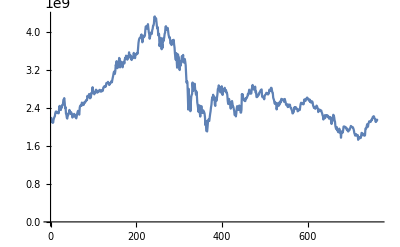

```mathematica
ListLinePlot[twapsWethUsdc90dFiltered2HourCandle, PlotRange->All]
```

```mathematica
Length[twapsWethUsdc90dFiltered2HourCandle]
```

762

```mathematica
twapsWethUsdc90dFiltered4HourCandle = Table[twapsWethUsdc90dFiltered[[i]], {i, 1, Length[twapsWethUsdc90dFiltered], 24}]
```

{2.20799×10^9,2.11006×10^9,2.12948×10^9,2.15282×10^9,2.20923×10^9,2.28598×10^9,2.327×10^9,2.31566×10^9,2.2911×10^9,2.28924×10^9,2.44522×10^9,2.39108×10^9,2.43401×10^9,2.45836×10^9,2.48836×10^9,2.58211×10^9,2.5154×10^9,2.41881×10^9,2.25792×10^9,2.17754×10^9,2.24668×10^9,2.30586×10^9,2.31699×10^9,2.27259×10^9,2.28115×10^9,2.19895×10^9,2.24249×10^9,2.27615×10^9,2.2202×10^9,2.19508×10^9,2.22228×10^9,2.31413×10^9,2.31663×10^9,2.2594×10^9,2.44623×10^9,2.46507×10^9,2.51503×10^9,2.48933×10^9,2.46433×10^9,2.51242×10^9,2.52488×10^9,2.55165×10^9,2.56814×10^9,2.63722×10^9,2.62802×10^9,2.63928×10^9,2.61809×10^9,2.71902×10^9,2.71774×10^9,2.73414×10^9,2.71973×10^9,2.72397×10^9,2.76668×10^9,2.77752×10^9,2.72296×10^9,2.75368×10^9,2.75674×10^9,2.78216×10^9,2.74595×10^9,2.76471×10^9,2.75652×10^9,2.82967×10^9,2.85625×10^9,2.84947×10^9,2.85328×10^9,2.92361×10^9,2.93936×10^9,2.91731×10^9,2.88564×10^9,2.9166×10^9,2.94487×10^9,2.94192×10^9,3.03939×10^9,3.13349×10^9,3.16459×10^9,3.17997×10^9,3.28365×10^9,3.31206×10^9,3.35822×10^9,3.35429×10^9,3.4358×10^9,3.36501×10^9,3.29343×10^9,3.29762×10^9,3.35215×10^9,3.37133×10^9,3.42208×10^9,3.44475×10^9,3.48886×10^9,3.41839×10^9,3.49581×10^9,3.57419×10^9,3.46529×10^9,3.48685×10^9,3.41145×10^9,3.45631×10^9,3.49927×10^9,3.52548×10^9,3.45079×10^9,3.53249×10^9,3.53244×10^9,3.54691×10^9,3.7727×10^9,3.86521×10^9,3.88178×10^9,3.93227×10^9,3.88966×10^9,3.83344×10^9,3.88842×10^9,3.90845×10^9,4.05106×10^9,4.10294×10^9,4.1261×10^9,4.16758×10^9,4.00082×10^9,3.86068×10^9,3.94848×10^9,3.99749×10^9,4.04201×10^9,4.13384×10^9,4.18279×10^9,4.32988×10^9,4.25303×10^9,4.20803×10^9,4.07428×10^9,3.93195×10^9,3.95475×10^9,3.75988×10^9,3.87894×10^9,3.63904×10^9,3.66591×10^9,3.80587×10^9,3.88821×10^9,3.98888×10^9,4.12435×10^9,4.04564×10^9,4.08866×10^9,3.94742×10^9,3.88051×10^9,3.8112×10^9,3.80199×10^9,3.82092×10^9,3.82047×10^9,3.83784×10^9,3.67614×10^9,3.47452×10^9,3.55881×10^9,3.2503×10^9,3.53029×10^9,3.46885×10^9,3.20058×10^9,3.28975×10^9,3.38069×10^9,3.49063×10^9,3.51933×10^9,3.36827×10^9,3.43181×10^9,3.30036×10^9,2.93567×10^9,2.94925×10^9,2.36736×10^9,2.61962×10^9,2.55795×10^9,2.51589×10^9,2.67406×10^9,2.93724×10^9,2.76519×10^9,2.78922×10^9,2.80395×10^9,2.68311×10^9,2.67897×10^9,2.46356×10^9,2.31838×10^9,2.45616×10^9,2.21985×10^9,2.43979×10^9,2.34224×10^9,2.30329×10^9,2.30606×10^9,2.28093×10^9,2.03948×10^9,1.91851×10^9,1.90531×10^9,2.11359×10^9,2.13307×10^9,2.20476×10^9,2.32941×10^9,2.46446×10^9,2.62629×10^9,2.67928×10^9,2.62988×10^9,2.47356×10^9,2.6091×10^9,2.55355×10^9,2.6901×10^9,2.80471×10^9,2.85532×10^9,2.75038×10^9,2.73084×10^9,2.8591×10^9,2.67599×10^9,2.75202×10^9,2.81068×10^9,2.78214×10^9,2.77527×10^9,2.72264×10^9,2.55426×10^9,2.48381×10^9,2.54233×10^9,2.47639×10^9,2.5117×10^9,2.54846×10^9,2.429×10^9,2.38374×10^9,2.25483×10^9,2.28777×10^9,2.28894×10^9,2.44064×10^9,2.4069×10^9,2.41598×10^9,2.43316×10^9,2.3045×10^9,2.36074×10^9,2.63788×10^9,2.59494×10^9,2.56346×10^9,2.54594×10^9,2.59317×10^9,2.60571×10^9,2.64567×10^9,2.68315×10^9,2.78665×10^9,2.75045×10^9,2.702×10^9,2.8057×10^9,2.88601×10^9,2.79149×10^9,2.7951×10^9,2.85143×10^9,2.74784×10^9,2.62981×10^9,2.65359×10^9,2.69806×10^9,2.72595×10^9,2.76066×10^9,2.78586×10^9,2.65956×10^9,2.64143×10^9,2.62734×10^9,2.64994×10^9,2.68312×10^9,2.72154×10^9,2.69476×10^9,2.685×10^9,2.71029×10^9,2.77828×10^9,2.75931×10^9,2.82294×10^9,2.72537×10^9,2.61717×10^9,2.56237×10^9,2.48588×10^9,2.50658×10^9,2.37037×10^9,2.50014×10^9,2.47285×10^9,2.46379×10^9,2.49398×10^9,2.52718×10^9,2.5722×10^9,2.5748×10^9,2.56923×10^9,2.53271×10^9,2.5499×10^9,2.46765×10^9,2.47741×10^9,2.41968×10^9,2.4363×10^9,2.47141×10^9,2.41865×10^9,2.39932×10^9,2.33974×10^9,2.28863×10^9,2.32021×10^9,2.41939×10^9,2.41322×10^9,2.38659×10^9,2.3825×10^9,2.33704×10^9,2.36812×10^9,2.36042×10^9,2.48487×10^9,2.50074×10^9,2.49405×10^9,2.47645×10^9,2.56483×10^9,2.556×10^9,2.5649×10^9,2.59209×10^9,2.61314×10^9,2.58794×10^9,2.55399×10^9,2.52737×10^9,2.51529×10^9,2.52804×10^9,2.51265×10^9,2.43198×10^9,2.42319×10^9,2.3838×10^9,2.42291×10^9,2.4392×10^9,2.39098×10^9,2.34206×10^9,2.36907×10^9,2.34276×10^9,2.3487×10^9,2.289×10^9,2.22957×10^9,2.20334×10^9,2.24788×10^9,2.23837×10^9,2.22888×10^9,2.24877×10^9,2.20945×10^9,2.17645×10^9,2.18765×10^9,2.1968×10^9,2.06409×10^9,2.12632×10^9,2.25775×10^9,2.21159×10^9,2.11309×10^9,1.97741×10^9,1.99989×10^9,1.93646×10^9,1.88782×10^9,1.96598×10^9,1.88158×10^9,1.77392×10^9,1.90558×10^9,1.8817×10^9,2.00821×10^9,2.00925×10^9,2.00207×10^9,1.98614×10^9,1.94099×10^9,1.91134×10^9,1.92311×10^9,1.93889×10^9,1.99017×10^9,2.01498×10^9,1.99599×10^9,1.987×10^9,1.93112×10^9,1.8507×10^9,1.81803×10^9,1.8411×10^9,1.82119×10^9,1.73026×10^9,1.79042×10^9,1.76299×10^9,1.76902×10^9,1.87626×10^9,1.86664×10^9,1.85408×10^9,1.8269×10^9,1.82609×10^9,1.96833×10^9,2.01868×10^9,1.99984×10^9,2.07186×10^9,2.12203×10^9,2.10566×10^9,2.1202×10^9,2.14671×10^9,2.20963×10^9,2.22795×10^9,2.18074×10^9,2.15493×10^9,2.1508×10^9,2.15469×10^9}

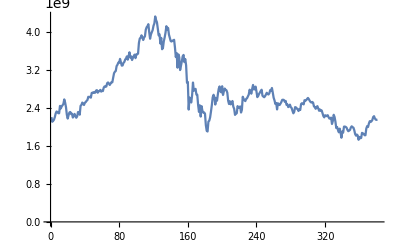

```mathematica
ListLinePlot[twapsWethUsdc90dFiltered4HourCandle, PlotRange->All]
```

```mathematica
Length[twapsWethUsdc90dFiltered4HourCandle]
```

381

```mathematica
twapsWethUsdc90dFiltered6HourCandle = Table[twapsWethUsdc90dFiltered[[i]], {i, 1, Length[twapsWethUsdc90dFiltered], 36}]
```

{2.20799×10^9,2.09635×10^9,2.15282×10^9,2.2252×10^9,2.327×10^9,2.30039×10^9,2.28924×10^9,2.41306×10^9,2.43401×10^9,2.45963×10^9,2.58211×10^9,2.39695×10^9,2.25792×10^9,2.27401×10^9,2.30586×10^9,2.31129×10^9,2.28115×10^9,2.22182×10^9,2.27615×10^9,2.23764×10^9,2.22228×10^9,2.34076×10^9,2.2594×10^9,2.45375×10^9,2.51503×10^9,2.50156×10^9,2.51242×10^9,2.55383×10^9,2.56814×10^9,2.63619×10^9,2.63928×10^9,2.62146×10^9,2.71774×10^9,2.73961×10^9,2.72397×10^9,2.78625×10^9,2.72296×10^9,2.74219×10^9,2.78216×10^9,2.7459×10^9,2.75652×10^9,2.84274×10^9,2.84947×10^9,2.92512×10^9,2.93936×10^9,2.89507×10^9,2.9166×10^9,2.96885×10^9,3.03939×10^9,3.16742×10^9,3.17997×10^9,3.38782×10^9,3.35822×10^9,3.45623×10^9,3.36501×10^9,3.36104×10^9,3.35215×10^9,3.33777×10^9,3.44475×10^9,3.47733×10^9,3.49581×10^9,3.506×10^9,3.48685×10^9,3.45358×10^9,3.49927×10^9,3.50502×10^9,3.53249×10^9,3.5612×10^9,3.7727×10^9,3.8787×10^9,3.93227×10^9,3.78543×10^9,3.88842×10^9,3.92922×10^9,4.10294×10^9,4.08194×10^9,4.00082×10^9,3.90141×10^9,3.99749×10^9,4.06711×10^9,4.18279×10^9,4.29344×10^9,4.20803×10^9,4.101×10^9,3.95475×10^9,3.76666×10^9,3.63904×10^9,3.86848×10^9,3.88821×10^9,4.1101×10^9,4.04564×10^9,4.02976×10^9,3.88051×10^9,3.75383×10^9,3.82092×10^9,3.81438×10^9,3.67614×10^9,3.41376×10^9,3.2503×10^9,3.47397×10^9,3.20058×10^9,3.33485×10^9,3.49063×10^9,3.36171×10^9,3.43181×10^9,3.11368×10^9,2.94925×10^9,2.8034×10^9,2.55795×10^9,2.63982×10^9,2.93724×10^9,2.79091×10^9,2.80395×10^9,2.74915×10^9,2.46356×10^9,2.41079×10^9,2.21985×10^9,2.43602×10^9,2.30329×10^9,2.31402×10^9,2.03948×10^9,1.92022×10^9,2.11359×10^9,2.12698×10^9,2.32941×10^9,2.56853×10^9,2.67928×10^9,2.63664×10^9,2.6091×10^9,2.62326×10^9,2.80471×10^9,2.83752×10^9,2.73084×10^9,2.72499×10^9,2.75202×10^9,2.82639×10^9,2.77527×10^9,2.67653×10^9,2.48381×10^9,2.49829×10^9,2.5117×10^9,2.49615×10^9,2.38374×10^9,2.25227×10^9,2.28894×10^9,2.41287×10^9,2.41598×10^9,2.38925×10^9,2.36074×10^9,2.68763×10^9,2.56346×10^9,2.54766×10^9,2.60571×10^9,2.69869×10^9,2.78665×10^9,2.70339×10^9,2.8057×10^9,2.82326×10^9,2.7951×10^9,2.72433×10^9,2.62981×10^9,2.65819×10^9,2.72595×10^9,2.77716×10^9,2.65956×10^9,2.62747×10^9,2.64994×10^9,2.69257×10^9,2.69476×10^9,2.70694×10^9,2.77828×10^9,2.82688×10^9,2.72537×10^9,2.59071×10^9,2.48588×10^9,2.47676×10^9,2.50014×10^9,2.44831×10^9,2.49398×10^9,2.59411×10^9,2.5748×10^9,2.53427×10^9,2.5499×10^9,2.46221×10^9,2.41968×10^9,2.45647×10^9,2.41865×10^9,2.36311×10^9,2.28863×10^9,2.40632×10^9,2.41322×10^9,2.38012×10^9,2.33704×10^9,2.35666×10^9,2.48487×10^9,2.49041×10^9,2.47645×10^9,2.58343×10^9,2.5649×10^9,2.62044×10^9,2.58794×10^9,2.57857×10^9,2.51529×10^9,2.53898×10^9,2.43198×10^9,2.40619×10^9,2.42291×10^9,2.40859×10^9,2.34206×10^9,2.33696×10^9,2.3487×10^9,2.24882×10^9,2.20334×10^9,2.18767×10^9,2.22888×10^9,2.23722×10^9,2.17645×10^9,2.21032×10^9,2.06409×10^9,2.17697×10^9,2.21159×10^9,2.01738×10^9,1.99989×10^9,1.90045×10^9,1.96598×10^9,1.88938×10^9,1.90558×10^9,1.9301×10^9,2.00925×10^9,1.99268×10^9,1.94099×10^9,1.90495×10^9,1.93889×10^9,2.02226×10^9,1.99599×10^9,1.96337×10^9,1.8507×10^9,1.85048×10^9,1.82119×10^9,1.7683×10^9,1.76299×10^9,1.82361×10^9,1.86664×10^9,1.83623×10^9,1.82609×10^9,1.97318×10^9,1.99984×10^9,2.0951×10^9,2.10566×10^9,2.15734×10^9,2.20963×10^9,2.22029×10^9,2.15493×10^9,2.12244×10^9}

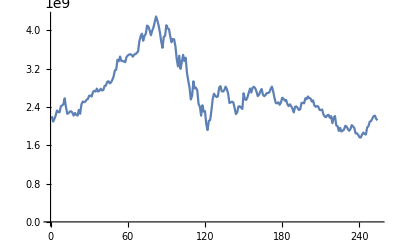

```mathematica
ListLinePlot[twapsWethUsdc90dFiltered6HourCandle, PlotRange->All]
```

```mathematica
Length[twapsWethUsdc90dFiltered6HourCandle]
```

254

```mathematica
(* Estimate distributional params for each candle set *)
```

```mathematica
edistWethUsdc90dFiltered
```

StableDistribution[1,1.46465,-0.0496207,-0.000010553,0.00154277]

```mathematica
rsWethUsdc90dFiltered30MinCandle = Differences[Log[twapsWethUsdc90dFiltered30MinCandle]]
```

{-0.00109063,-0.000203463,-0.0033752,-0.00601824,-0.00853513,-0.0156612,-0.0145234,0.00404176,-0.0049755,-0.0097474,0.00133791,0.00686793,0.00730924,0.00723779,0.00525786,-0.00412941,-0.00727048,-0.0120332,-0.00612722,0.00767391,0.0139255,0.00884889,0.00311192,0.00277306,0.00963267,0.00602424,0.000973497,-0.00225827,-0.00223694,0.00607323,0.0102374,-0.00257897,-0.0134094,-0.00767814,0.0108319,0.0174568,0.0120671,0.00592705,0.00730905,0.00164723,0.00406295,0.00832727,0.000814122,0.000647421,0.00696204,0.00189534,-0.00427618,-0.000649038,0.00227261,0.0036374,-0.0101629,-0.00484458,0.00466467,0.00106007,0.00276401,-0.00427674,-0.00670526,-0.000214317,0.00196614,-0.00166065,0.00256816,0.00346585,-0.00544219,-0.0046385,-0.00219709,0.00287972,0.00346312,-0.00057246,-0.00805607,-0.00660131,-0.00312222,0.0133926,0.0262695,0.00819415,0.00276601,0.00502215,0.0144554,0.00414703,0.00399314,0.00106935,-0.00515823,-0.00377044,-0.00153006,-0.00278237,0.00543793,0.00157293,-0.00720475,-0.0089559,0.000483714,-0.00162308,-0.006536,-0.006156,0.000808948,-0.000448454,0.0165035,0.0147627,-0.0130487,-0.00575194,0.0108058,-0.003756,0.00190664,0.00880533,0.00326081,0.00773193,0.0091359,-0.00339168,-0.00212333,-0.00310623,-0.00738275,0.00157113,0.0111178,0.0063077,0.00717053,0.0122196,0.0092808,0.00528814,-0.00157912,-0.00086144,-0.000825344,0.00628916,0.00387693,0.00280782,0.0100556,-0.00640689,-0.0217469,-0.00316935,-0.00322593,-0.00836505,-0.000863692,-0.0220131,-0.026571,0.00121265,0.00849206,-0.00156951,0.003466,-0.00130976,-0.00190523,-0.00871888,-0.020949,-0.0268626,-0.0278928,0.00958031,0.0100494,-0.00213378,-0.0120181,-0.011615,0.00460586,-0.00981603,0.00139763,-0.00702915,-0.0149412,0.0131667,0.00808359,0.00307893,0.0209664,0.0112192,0.00597366,0.00081406,-0.00916497,-0.00971087,-0.00876255,0.0133178,0.0108518,0.00305645,0.014414,0.00455682,-0.00324092,-0.00819297,0.00641056,0.0102273,0.00192412,0.00458732,-0.00253216,-0.00401967,-0.00473192,-0.00705367,0.00292296,0.006152,0.00439361,-0.0159304,-0.0200139,0.0050641,-0.006975,0.00504126,0.0144101,0.0011543,-0.000371742,0.00185784,-0.000568787,0.00299406,-0.00481461,-0.0109051,-0.00262278,0.00391583,0.00273932,-0.00751748,-0.00661115,-0.0113258,-0.0111259,-0.00415131,-0.00112543,0.00855579,0.00547407,-0.00255654,-0.00601178,-0.00346584,0.00373545,0.0150049,0.00319015,-0.00496349,-0.00233181,0.0127292,0.00717862,-0.000884306,-0.00127114,0.00124966,0.00565913,-0.0000227038,-0.00339345,-0.00772878,-0.00478803,-0.00761624,-0.00422619,-0.00277005,0.00579418,0.00393056,0.00089625,-0.002798,-0.0111727,-0.00911049,-0.00194039,0.00301894,0.00251823,-0.0000992836,-0.00352707,-0.00466422,0.00228831,0.00612088,0.00897367,0.000703148,0.014243,0.008136,-0.00234168,0.00468994,0.00924012,0.00523164,0.0019934,-0.0006916,0.00316766,0.00794283,0.0020892,-0.00175672,0.000724717,-0.000858844,-0.00481819,-0.00540736,-0.0073738,-0.0000999339,-0.00559733,-0.00447303,-0.0144635,-0.0146332,0.0052709,0.0163548,0.00920825,0.00777226,0.0256725,0.020613,0.00611954,0.00946281,-0.000298801,0.000900051,0.00199369,0.00285458,0.00249814,-0.00427993,-0.000296129,0.00707816,0.00426587,-0.00644583,-0.00389478,-0.00388906,-0.00180437,0.000689122,0.0116245,0.00618968,0.00344832,0.00770282,-0.000289982,-0.00414254,-0.00390698,0.00190506,-0.00297541,-0.00139843,0.00274917,-0.00221103,-0.00260151,0.0100355,0.00249266,-0.00502786,-0.00271491,-0.00159702,-0.00277736,-0.0079032,-0.00411378,0.0154392,0.00935999,0.00044402,0.00182364,0.000430145,-0.00407261,0.0000135126,0.000950282,0.0026291,0.000881473,-0.00612849,-0.0042839,0.000603005,0.00432072,0.00597597,0.00579232,0.00575827,0.00148251,-0.00163083,-0.00148823,-0.000673486,-0.000209272,0.00151435,-0.000539807,0.000125898,0.00366059,0.00462692,-0.0000686402,-0.00312986,-0.00285361,0.00462326,0.0178943,0.0080319,0.00606581,0.00220372,-0.00456877,-0.00232751,-0.000706817,-0.000052066,-0.000362454,-0.00456035,0.00188787,0.00264532,0.000734051,6.80786×10^-7,-0.00394529,0.000108251,0.00858806,0.0105645,0.00285197,0.00345444,0.00231098,-0.00775177,-0.0113933,-0.0043525,0.00133662,-0.00139049,-0.00384605,-0.00944197,-0.00752728,0.00491573,0.00561988,0.00227336,-0.00132224,-0.00557243,0.00255882,0.00562482,0.00936889,0.0141213,0.00895195,0.00409439,-0.00637545,-0.00117246,0.00516724,-0.00271589,-0.00796258,0.00198167,0.00609456,0.00451536,0.000669955,0.00319111,-0.000149349,0.0398486,-0.0406213,-0.00459108,-0.00059742,0.00826568,0.00318311,-0.00721968,0.000361711,0.00567292,0.00067986,-0.00534524,-0.00403208,0.00141323,0.00023089,-0.00150938,-0.00506701,-0.00508939,0.000177815,0.00354346,0.004805,0.00446492,0.00218372,0.00048885,-0.00180405,-0.00297079,0.00675092,0.00997598,0.00037613,0.000556881,0.000501301,-0.000309052,0.00484297,0.0020134,-0.00505767,-0.00315224,0.00113301,0.00394011,0.00212833,-0.00644858,-0.0088168,-0.00221859,-0.0047088,-0.00227689,0.00325699,-0.000752818,-0.00456082,-0.000480397,0.000993257,0.0077801,0.0073125,0.00298318,0.0000203458,-0.00283056,-0.00339276,-0.0022346,0.0019982,-0.0005528,-0.000692031,0.000291155,0.00222994,0.00346201,0.00190035,0.000951951,0.00211284,0.00387894,0.000438802,-0.00179266,-0.0012444,0.00293239,0.00225094,-0.00735918,0.00370287,-0.00544354,-0.0044067,-0.00258357,0.00155729,-0.000816464,-0.00087544,0.00355333,-0.000949143,-0.00174885,0.000298117,0.00206343,0.00331243,0.00115363,0.000171305,0.0000405473,0.00340787,0.00117139,-0.00206882,-0.00265119,-0.00258781,-0.000449961,-0.00130772,0.000247524,0.00344245,0.00266946,-0.000249461,-0.00076173,0.00889988,0.0132516,0.000526295,0.00216827,0.00226979,-0.000356306,0.00265936,0.00420882,-0.00236474,0.000235914,0.0000867426,-0.000120049,0.000541732,-0.00644394,-0.00218069,0.00130836,0.000199918,0.00423366,0.00200847,0.00417892,0.00233024,-0.00135155,-0.000484533,-0.000886581,-0.00274197,-0.00171623,0.0057345,0.0064192,0.00751254,0.00520045,0.00204898,0.000764611,-0.00127507,-0.00205604,0.00361772,0.00130644,-0.00325648,0.00108133,0.00201578,0.00209398,0.000541263,-0.00202819,-0.00122549,0.00045418,0.00283153,0.00201795,-0.00246858,-0.0106824,-0.000310137,0.00185341,-0.000336661,0.000582216,-0.00277574,-0.00512262,-0.00348999,-0.00410519,0.00137221,0.00296081,0.00733059,0.00307104,-0.000386263,0.00219728,0.0024608,-0.000841048,-0.00126878,-0.00189118,0.000785578,-0.0359371,0.0379117,0.00289128,0.000696884,-0.000150622,0.00111188,0.00233549,0.00485599,0.00458882,0.000237888,-0.00157317,0.000250597,0.00147074,-0.00562104,-0.00521294,0.00153796,0.00701241,0.00644831,0.00190052,0.00550892,0.0029571,0.00243868,0.00479334,0.00441572,0.000280098,0.000659048,0.00800527,0.00409776,-0.000722902,0.00374817,0.0100055,0.00725201,0.00708424,-0.00314867,-0.000418386,-0.00413385,-0.00155267,0.00504594,-0.000253035,-0.00594972,-0.00329907,-0.00472374,-0.00033804,0.0102925,0.00589708,0.000442434,0.002527,0.0164765,0.0109732,0.00618232,0.00639574,-0.0000263908,-0.0040646,-0.00161752,-0.00223604,0.00110039,0.00446357,0.0172004,0.00846829,0.00847956,-0.00186815,-0.0154767,-0.0137514,-0.00353794,-0.00623345,-0.0103161,-0.00181317,0.00206531,0.00914982,0.015633,0.00889231,0.00393272,0.00180403,-0.00351896,-0.00378811,-0.00948658,-0.00495347,0.00820858,0.00663328,0.00428977,0.0113743,0.00626945,0.008002,-0.00157291,0.00516882,0.00600264,-0.0155248,-0.0116093,-0.0239035,-0.0112194,-0.00686263,0.00501739,0.0111509,0.00820301,0.00840363,0.00464137,0.00624873,-0.00390741,-0.00246993,-0.00891751,-0.0131284,-0.00541682,0.00144957,-0.0057142,0.00808902,0.0098811,0.00806287,-0.0021022,-0.00828499,-0.00846888,-0.000192131,-0.0016993,-0.00770945,0.00184109,-0.00452299,-0.00206392,0.00774783,0.0147726,0.00803515,-0.000490807,0.00329787,0.00490369,-0.0022466,-0.00152695,-0.00131394,0.00230104,0.000779669,0.00129858,-0.0082589,-0.00591427,0.0028716,-0.00479224,0.0104875,0.0195401,-0.000290315,-0.00326424,0.000377956,0.00410116,0.00851143,0.00217008,-0.0025729,-0.00241509,-0.000303999,0.0118038,0.00943544,0.00162678,-0.00573013,-0.00847791,-0.00132319,0.00269554,0.0026916,-0.00159988,-0.00399583,0.00274374,-0.00045656,-0.0072713,-0.00036548,-0.00374943,-0.00570912,0.00058079,0.00530305,0.00212646,-0.000370937,0.00266489,0.00636425,0.00367055,0.00205456,0.00389508,-0.00313896,-0.00322455,-0.00103899,0.00118274,0.00840609,0.0098651,0.00622844,0.000142361,0.000200706,-0.00231677,-0.0172904,-0.0167528,0.00313141,0.00212956,-0.000188291,0.005926,0.00743252,0.00374873,-0.00196487,-0.00556873,0.00189643,0.000582173,-0.00584946,-0.00471843,-0.00567204,-0.00540027,-0.00052528,-0.00583214,-0.00533578,0.00351188,0.00211059,0.00439677,0.00403352,0.00409006,-0.000246155,-0.00718749,0.000867956,0.00399442,0.00311754,0.00226625,-0.00219468,-0.000933793,-0.000950306,0.00372021,0.00875367,0.00306957,-0.00137978,-0.00132383,0.00400096,0.00976336,0.00526271,-0.00193075,0.000276864,-0.00414124,-0.00444632,-0.000621358,-0.00123581,0.000239256,-0.00420301,-0.00551334,0.0000873526,-0.00556032,-0.00460628,0.00477054,0.00486778,0.00588313,0.00648079,0.00382028,-0.00008238,-0.00175036,-0.000588554,0.00382677,0.00671379,-0.00252719,-0.00375783,-0.00183687,-0.00331339,-0.00123584,0.0021154,0.00637398,0.00312547,-0.0031993,0.00181051,-0.000660173,-0.00408034,0.000570472,0.000147172,0.00211435,0.00790483,0.013549,0.006688,0.00293511,-0.0237314,0.0337385,0.0185155,0.00916641,0.0039133,0.00120327,0.00112669,-0.00346134,0.00124594,0.00647059,0.00456,0.00919132,0.00197003,-0.00763971,-0.0000371234,0.00216096,-0.0055167,0.000745763,0.00340551,-0.00163219,0.00509381,0.00724677,-0.00773027,-0.00561982,0.00888206,0.00386468,0.00281722,0.00648735,0.000197284,-0.00214153,0.000126859,-0.00292629,-0.00588244,-0.0059871,-0.000770711,0.00486187,-0.00331123,-0.0159923,-0.0127197,-0.00179925,0.00751934,0.00409282,0.00279049,0.00182958,0.0135219,0.011802,-0.00366485,-0.00270063,0.000214321,-0.00233212,-0.00443088,-0.00404654,0.00367093,0.0059382,0.00143714,-0.00119648,-0.00265408,-0.00166779,0.00365789,0.00109515,-0.000896336,-0.000291246,0.00539157,0.00550539,0.00618585,0.0118196,0.00702626,0.00315897,0.0102673,0.000922458,0.00274276,0.000758502,-0.000778725,-0.00192818,-0.00241577,0.00712478,-0.0021962,-0.00429345,-0.00650889,-0.00936779,0.00266446,0.0102411,0.0079629,0.00260347,-0.0029435,-0.00743088,-0.00298902,0.00874767,0.0130778,0.000567831,-0.00162973,-0.00344696,-0.00410262,-0.00111231,-0.0117236,-0.033291,-0.0154233,0.0131384,0.0151246,-0.0379416,0.0324836,-0.00837998,0.00307674,-0.0101877,-0.00796931,0.00261838,-0.00935449,-0.010153,0.00335405,0.0100841,0.00720998,-0.00237816,0.000490385,0.0102372,0.00364175,-0.000382,-0.00317701,-0.000509955,0.00688073,0.0148662,0.00800574,-0.00132718,-0.0120197,-0.0125285,0.00119204,-0.00297442,0.00559809,0.00438206,0.00534783,0.00877082,0.00128733,-0.00450039,0.00261689,0.00738253,0.000691195,-0.00262484,0.0019607,0.00827151,0.00866662,-0.000536049,-0.00333141,0.00224899,0.00286267,0.0049918,0.00289999,0.000563635,0.00207167,0.0110693,0.00818315,0.00792668,0.00566026,-0.00340159,0.00336811,0.00289035,-0.00113359,-0.00350033,-0.00130721,-0.00376575,0.00012147,0.00197292,-0.00284673,-0.00641159,-0.00217133,0.00274211,0.0031026,0.00467719,-0.00242428,0.00118322,0.00920564,-0.0143733,-0.0147498,-0.0141934,-0.00146197,0.00308125,-0.00906305,-0.0190207,-0.0098826,0.0105018,0.00773705,0.00276802,0.005666,-0.00273437,0.00083678,-0.000488314,-0.0481773,-0.0178406,0.0244105,0.00479461,0.0102323,0.00421706,-0.00995272,-0.0119549,0.0049621,-0.00161549,0.0051009,0.0107081,0.000710703,0.00115144,-0.0777608,0.0644016,-0.0148984,-0.0193279,-0.0155151,-0.00668812,-0.0157744,0.0111252,0.0131388,0.011367,0.00268917,0.00990397,0.00541138,-0.0122878,-0.010456,0.00736394,-0.0190994,-0.0288734,0.00759011,-0.0075436,-0.000534315,0.00985059,0.00234555,0.00806915,0.00883286,-0.000170221,-0.00280408,-0.0116902,-0.0070783,0.0203134,0.0142634,0.0119977,0.00721118,-0.00737808,-0.00693652,-0.00203093,0.0000279882,-0.00142877,-0.00100597,0.00607451,0.00533269,-0.0051892,0.00562655,0.00825813,0.00373758,0.00778718,0.00978818,0.00255432,-0.000477132,0.00753943,0.00465017,-0.00352589,-0.00275568,0.0018532,0.00972227,0.0060424,0.0123199,0.00808244,-0.000948337,-0.00325135,-0.000421457,-0.00328075,-0.00518499,-0.00444122,-0.00270092,-0.00579068,-0.00748174,0.00358787,0.00602357,0.00799333,0.0022624,0.00194253,-0.00296864,-0.0063879,0.00765739,0.00285238,-0.00277375,-0.00623178,-0.00462393,-0.000490318,-0.00316563,-0.00437155,0.00151353,-0.00618255,-0.0116037,-0.00443256,-0.00292547,0.000807693,-0.0030972,-0.00893165,-0.00720019,0.00358317,0.00510174,0.00407435,0.00429703,-0.000848537,-0.00541955,-0.00218495,0.00473939,-0.00603096,-0.01665,-0.0150761,-0.000666573,0.00224515,-0.00167021,-0.00979919,0.000847081,0.0151089,0.0065907,0.000576941,0.00104304,-0.00588464,-0.0156245,-0.0113678,0.01662,0.010889,0.0087161,0.00184614,-0.000216675,-0.0039536,-0.00110177,0.00368341,-0.00265716,-0.00326961,0.00555149,0.0114484,-0.00345407,-0.00400255,-0.00558871,-0.00271169,0.00233797,0.00344781,0.00305838,0.000200506,-0.00550304,-0.00708465,-0.013289,-0.00847266,0.00173348,-0.0022336,-0.00839711,-0.00347941,-0.00477257,-0.0107494,-0.017611,0.00620252,0.00761134,-0.0179348,-0.0156756,-0.00849011,-0.0080638,-0.00889238,0.00780582,0.0256632,0.0107274,-0.000140057,0.00536168,-0.00152536,-0.0107216,-0.0224099,-0.0055569,-0.00139776,-0.00979022,-0.0183313,-0.0209479,0.0080128,0.00600784,-0.000665185,0.0255127,0.0119433,0.0125806,0.0118783,0.00736351,-0.00171135,-0.00402657,-0.00150431,-0.00883859,0.00299957,0.00932952,-0.00459139,-0.00921276,-0.00530481,-0.011609,-0.00851609,-0.00991329,-0.0146597,-0.0100243,-0.0212078,0.000743722,0.0205992,0.0249723,0.00758167,0.00189061,0.0123464,-0.00191257,-0.0233569,-0.0146404,-0.013518,0.000691566,0.0142449,0.0121953,0.00804751,0.00627479,0.000321267,-0.000990256,0.00377972,0.00163942,0.0116101,0.0156833,0.00989385,0.00261881,-0.00287665,-0.0103452,0.00186855,0.00293712,-0.00561429,-0.00649432,0.00135206,0.00564139,0.00363134,0.00486441,-0.00394955,-0.0175117,-0.0134531,-0.0109061,-0.0181577,0.00767557,0.0131039,-0.000670881,0.0098213,0.00563923,-0.00805564,-0.00807349,-0.0290842,0.0330781,0.00857298,0.00678831,0.00269967,-0.00843434,-0.00252895,-0.00888682,-0.00242287,0.0104578,-0.00335356,-0.0265848,-0.02517,-0.00965676,-0.0145366,-0.00886523,-0.0052805,-0.0362232,-0.0122791,-0.00508445,0.0106289,0.00105904,-0.0124885,0.00962466,-0.000187303,0.00410979,0.000509196,-0.00864224,-0.0160436,-0.0311355,-0.0444262,-0.00549436,-0.0700061,-0.14464,0.026722,0.0652501,0.0395418,0.064485,0.0283681,0.0366611,0.0143253,-0.0328611,-0.0371037,-0.0121646,0.00168641,0.00605532,-0.0257083,-0.0203697,0.0245188,0.0279573,-0.00451912,-0.0334425,-0.03076,-0.0655681,-0.0299977,0.0342253,0.02924,0.0202069,0.00785448,0.0182163,0.0369644,0.000718716,0.00575232,0.00465041,0.0227767,0.0111231,-0.00963624,-0.0113767,-0.0114338,0.00811244,0.00754094,0.0049691,0.0117168,0.0292802,0.0346049,0.0090819,-0.0056487,0.0002702,0.00128969,-0.0291924,-0.0495218,-0.00157709,0.0127941,0.0112236,0.00859471,0.00320646,0.00381478,-0.00635586,-0.00384602,0.0137692,-0.00777703,-0.00275225,-0.00117853,0.00821488,0.0241801,0.0115159,-0.00459374,-0.0101751,-0.0110131,-0.0116828,-0.007493,-0.00467699,0.000189722,-0.00832062,-0.00375185,0.00118938,-0.0137625,-0.0074271,0.00637682,0.013828,0.00593613,-0.00182622,-0.0150433,-0.00849562,0.00641067,-0.0087318,0.00354193,0.00451912,-0.047296,-0.0235831,-0.0148211,-0.0110047,0.00881975,-0.00399945,-0.00156631,-0.00753914,0.00082855,-0.0222576,-0.026002,-0.0177324,-0.0228222,0.0363528,0.0259609,0.00851915,0.00391379,0.000692504,0.00316562,0.00969072,0.00488989,0.000896409,-0.0141544,-0.0224154,-0.0150048,-0.020172,-0.0225828,-0.00903656,0.000938331,0.00127024,0.00120725,0.0160382,0.0315143,0.00349288,0.00277078,0.00272711,0.0235924,0.0131301,-0.00880981,0.00272992,-0.00308557,0.00761928,0.00110267,-0.0220508,-0.020132,0.00182126,0.009561,-0.000410035,-0.0141825,-0.0151006,-0.00409937,0.00316937,0.00301106,0.00128142,0.0150679,0.00815157,0.00211259,-0.00507259,-0.00417073,0.000988663,-0.0151342,-0.000740712,0.0184919,0.00624136,-0.00818325,-0.0131058,-0.00484552,0.00521337,-0.00580319,-0.00896924,-0.0152191,-0.00483394,-0.00631464,-0.0084011,-0.0110043,-0.0181403,-0.0269006,-0.021073,-0.00862153,0.0249972,0.0281924,-0.00182685,-0.00552757,-0.0313076,-0.052376,-0.014674,0.0110693,0.009605,-0.00196236,-0.0178212,-0.0414129,-0.00713216,0.0476661,-0.00691803,-0.00511197,0.00987994,0.0201455,0.0238517,0.0262522,0.0214854,0.0038078,0.00343324,-0.0089056,-0.00266315,0.0131416,0.0194772,-0.00726058,-0.0103992,0.00324909,0.00253648,0.0148268,0.0000350951,-0.0111496,-0.00657153,0.000767632,-0.00194403,0.010074,0.0270157,0.0267367,0.00950725,-0.00187777,-0.00314951,-0.00662469,-0.00266058,0.00657018,0.0264967,0.0241475,0.0122125,-0.00838599,0.00759137,0.00600456,0.0140098,0.0118846,-0.0111089,0.000848845,0.0132417,0.0189926,0.00827889,-0.0047005,0.0184851,0.00706032,0.00139522,0.00374859,-0.0135413,-0.00184346,0.00136945,0.0165915,0.0247458,0.00449058,-0.0155848,-0.0151067,-0.0139427,-0.0121874,0.00442788,-0.00255853,0.00206469,-0.00161412,0.0203066,0.00483818,0.00630978,-0.00289548,-0.00568503,-0.013502,-0.0103033,-0.0129551,-0.0270862,-0.0113708,0.000653938,-0.00510995,0.00407275,0.0234276,0.0200304,0.0193009,0.0023397,-0.00720808,-0.00171146,-0.00203378,-0.00335436,0.000198193,0.00929903,-0.00502497,-0.0116832,-0.00428145,0.00350565,0.00789013,0.0198158,0.0233375,0.00718377,-0.00177864,-0.00358171,-0.00334056,0.0117129,0.0177582,0.0147782,0.00201513,0.00542889,-0.00301547,-0.00361522,0.00477566,0.000323288,0.0109826,0.00964137,-0.000670886,-0.00346927,-0.00300001,-0.000697643,-0.00875504,-0.00857985,0.00226097,0.00881821,0.00468844,-0.0176318,-0.0206866,0.00243872,-0.00160154,-0.0035503,0.00815718,-0.0110801,-0.0110378,0.00626135,0.00606844,-0.00034485,-0.00247525,0.00929143,0.0150043,0.00258428,0.00397434,0.00541843,0.00309686,0.00900066,-0.00195445,-0.0154508,-0.0146603,-0.0159758,-0.00448353,-0.00865541,-0.00698075,0.00197684,0.00326736,0.000877356,0.00613986,0.00871349,0.00474601,0.00126759,-0.00278046,0.00578142,0.0096645,0.00392954,0.00110947,0.000496814,0.00320591,0.00585877,-0.00296915,-0.00020239,0.00939839,0.00430633,0.00179674,-0.00992795,-0.00847114,-0.00578415,-0.00322112,0.00169679,0.00180346,-0.000712646,-0.00432067,-0.00702824,-0.00118363,-0.00650364,0.00475004,0.0107223,-0.00137343,-0.00550774,-0.00576909,-0.00626469,-0.00177075,-0.0075057,0.00525115,0.00379539,0.00014891,-0.00209642,-0.00507209,-0.0100634,-0.00412851,-0.016991,-0.0244876,-0.00115233,0.00396375,-0.0012147,-0.00736428,-0.0216213,-0.00419624,0.00731226,0.00268049,-0.00752691,-0.00193519,0.0207459,0.0181091,0.00589953,-0.00642167,-0.00710834,0.00033281,-0.00633673,-0.0134311,-0.00445723,-0.00026791,0.000683961,0.00872454,-0.00136637,-0.00436479,-0.0117988,-0.0316468,-0.013879,0.00504349,0.00368837,0.00897744,0.00986326,0.0138097,0.0183024,0.00522218,-0.00388653,-0.00175312,0.00431379,0.000424111,-0.00407348,0.0010291,0.0132538,0.000194223,-0.00388832,-0.00765709,-0.0093893,-0.00869969,-0.0114628,-0.00830723,0.00120079,-0.000488715,-0.00239739,0.0051261,-0.00228383,-0.0117408,-0.0113575,0.00434114,-9.85842×10^-6,-0.0181906,-0.00931327,0.00442701,0.00711958,-0.0150455,-0.016878,-0.00221634,-0.00549953,-0.00348254,-0.0049615,0.00150142,0.00580695,0.00586205,0.000519606,0.00344327,0.00581368,-0.020029,-0.0111848,0.000501631,0.00215497,0.0123348,0.0122497,0.00379068,0.000696518,0.00448308,0.0121943,0.0171382,0.0114201,0.00973776,0.00591339,0.00469967,-0.00141626,-0.00311964,-0.00188462,-0.00429817,-0.00214289,-0.000229112,0.00371594,0.00583626,-0.0117995,-0.00733013,-0.000419377,-0.00799528,-0.0043102,0.00211593,0.00753401,0.00908432,0.00508806,0.00541239,0.00526591,0.00585139,-0.00118636,-0.00348688,-0.000700405,-0.00253017,-0.00153999,-0.00470133,-0.00713508,-0.00454039,-0.00183521,-0.0078663,-0.00975829,-0.0123714,-0.0061193,0.000908202,-0.000639589,-0.000164866,-0.00110564,0.00210191,0.00655353,0.00578413,0.0106707,0.018377,0.07112,0.0527661,-0.0104138,-0.0142186,-0.00663016,0.0047389,-0.00473678,0.000508345,0.00488376,0.00987169,0.00341906,-0.00916286,-0.00333493,-0.00608124,-0.0165157,-0.0072401,-0.000923579,0.00309594,0.00708316,0.00496101,-0.000560642,-0.0101414,-0.00848163,0.0138052,0.00968859,-0.00928032,-0.0109167,-0.00290558,-0.000145773,-0.00574123,-0.00136289,0.00535775,0.00322349,-0.00369239,-0.00420996,0.00436355,0.00500328,-0.0025897,0.0109272,-0.000249161,0.00327234,0.00991183,-0.00521802,-0.0107356,-0.00643467,0.00727884,0.00699644,0.00519176,0.00156953,0.00151374,0.000575323,-0.00246383,0.00362687,0.00374037,0.00146703,0.0206421,-0.00378818,0.000196114,0.00279315,-0.00162902,-0.00136206,-0.0737889,0.0710032,0.00510767,0.00321646,-0.00125656,0.00735031,0.00507131,0.00646718,0.00849695,0.00339504,-0.00302589,-0.00492949,-0.00151749,0.0015814,-0.0000675167,-0.000100268,-0.00163675,-0.00337875,-0.00803781,-0.000943279,-0.00184866,-0.00642855,-0.00170185,0.00454418,-0.00265228,-0.000705524,-7.19434×10^-6,-0.00527003,0.00130822,0.00623943,0.00707048,0.0103936,0.00976062,0.00816606,0.00616966,0.00443343,-0.00376166,0.00123811,0.00333493,0.0034444,0.00831215,0.00505112,-0.00738467,-0.0111377,-0.00789832,0.00443775,-0.000584406,-0.00995959,-0.00330256,0.00253198,0.00257767,-0.00165019,0.00689364,0.00642739,0.00120511,-0.00300699,-0.00624097,-0.00491537,-1.04934×10^-6,0.00177522,0.0053066,0.00487169,-0.000917785,0.00340258,0.00514464,0.000370486,-0.0100817,-0.0116299,-0.0179182,-0.00596532,0.00248137,0.00627373,0.00407353,-0.00423822,-0.0106908,-0.0157696,-0.00536673,-0.0109601,-0.00547758,0.00311568,0.00200604,-0.000759681,0.00418072,0.00376703,-0.00355946,-0.00206971,-0.0100107,-0.00344066,0.016197,0.00393916,-0.00621351,-0.000798656,0.00453692,0.00420548,0.00453116,-0.000759469,0.00830185,0.00281308,-0.00109223,0.0021133,-0.00346022,-0.000905506,0.00463318,0.00728913,0.00204054,-0.000331429,-0.00538692,-0.00872243,0.00553065,0.0140979,0.007599,0.00141503,-0.000224863,-0.00165656,0.00208586,0.000311737,0.00156682,0.00199356,-0.000860558,-0.00160317,0.00215798,0.00343452,0.00420055,-0.00142406,0.00304291,-0.00356472,-0.0208655,-0.00815657,-0.00473166,-0.0148964,-0.00752771,0.000078914,-0.00198727,-0.00317716,-0.00335164,-0.00362452,0.00691902,0.00582724,-0.00385095,-0.00155118,-0.000394566,0.000499658,0.000918939,-0.00191568,-0.00103303,0.00198028,-0.0103707,-0.0116432,0.00318641,0.00237301,0.0059681,0.00818908,0.00327601,0.00758781,0.00812412,0.0045619,-0.000472106,-0.00264118,0.000656105,0.00168395,-0.000114797,0.000641758,-0.00124455,-0.00558042,0.00282738,0.00751646,0.00651933,0.00556507,0.00183778,-0.00322019,-0.00327105,-0.0016325,-0.00157237,-0.000594834,-0.00438256,-0.00702276,-0.000911321,0.00949876,0.00852056,0.00179169,0.00129238,-0.00302279,-0.00592307,-0.00386024,-0.00111618,-0.00131213,-0.0016749,0.00103749,0.00514478,0.0036322,-0.00333928,-0.00327562,0.00302402,0.00482709,0.0103885,0.00620519,0.00370915,0.00751408,0.00201192,-0.000816047,-0.00468134,0.00044508,-0.000419164,-0.000257624,0.00133461,-0.000954935,-0.0064032,-0.000509523,0.000911124,-0.000552567,0.0040639,0.0083552,0.0102225,0.00154893,-0.00274958,-0.00162481,0.00497622,-0.00199588,-0.00926449,-0.00621035,-0.00203996,0.00157162,-0.000570373,-0.00332846,-0.00831375,-0.00701887,-0.00577792,-0.00400793,0.0013708,0.00640256,-0.00479095,-0.0219078,-0.0155877,0.0037877,0.00154167,-0.00280648,-0.00557532,-0.00332096,-0.00114054,0.00598231,-0.000819968,-0.0150212,-0.0281601,-0.00455937,0.0101425,0.000349025,-0.00591672,-0.00152854,0.00176311,-0.00239606,0.00700566,0.00892304,0.00580908,-0.00889976,-0.00605286,0.00033445,-0.00310272,0.00427634,0.011735,-0.00634637,-0.00804658,-0.00931097,-0.0214298,-0.0165616,-0.013776,0.0078622,0.0147838,-0.0000666107,-0.000406127,0.00845212,0.0134327,0.00571733,0.00523966,0.00614746,0.00982144,0.00132083,-0.00146949,-0.010063,0.0117882,-0.00225924,-0.00951466,-0.0105997,-0.00419119,-0.00542233,-0.00572981,0.00536962,0.00426142,-0.00600198,-0.00415291,0.0121982,0.00697475,0.00694948,0.0115594,-0.000181369,-0.00739823,-0.00570945,-0.000771226,0.00075518,0.000253203,0.00395853,0.00197991,0.0151358,0.00307594,-0.00667205,-0.00256496,-0.00194006,-0.00420068,0.0142189,0.00801585,0.00810352,0.00417794,-0.00455992,-0.00240913,-0.00569037,-0.00238875,-0.000870201,0.000875123,0.00239567,0.00796157,0.0108219,-0.00714556,-0.010639,0.00777068,-0.00305728,0.0021734,-0.00393098,-0.00467885,0.00252758,0.00148902,-0.00446002,-0.005123,-0.00501869,-0.00409776,0.000537383,0.00228253,0.00179092,-0.000199197,-0.00448951,-0.00669413,0.00849532,0.0174519,0.00343834,-0.00471537,-0.00479002,-0.00490828,-0.00151421,-0.00264572,-0.0030498,-0.00487985,-0.00156428,-0.00416462,-0.00676898,-0.00497925,-0.00473468,0.000228373,-0.000370687,-0.00101934,-0.00104514,-0.00642043,0.0014214,0.00696336,0.00419091,0.00349433,0.00174415,-0.00288663,-0.00436333,-0.0111057,-0.0101335,-0.000729628,0.00040137,0.00980383,0.00679298,0.00138351,0.00340412,0.00246347,-0.00259942,-0.0067509,-0.00765023,-0.00072587,0.00593612,0.00305267,-0.0000184393,0.00305337,0.0019922,0.00208639,-0.00107131,-0.00276408,-0.00254044,0.00164968,0.0030085,-0.000976298,-0.0050265,-0.00961917,-0.00530867,-0.00866707,-0.00589516,0.00542663,0.000791244,0.000817485,0.00348971,-0.00201685,-0.00197154,-0.0066096,-0.0131506,0.000493725,0.00406103,-0.00736683,-0.000812505,-0.000518995,-0.00124019,-0.00867311,-0.013164,-0.00568971,0.00439883,0.00276778,0.00103387,-0.00355535,0.000793213,0.000777914,0.000822168,0.00558107,0.00470626,0.0000999676,-0.000737234,0.00122783,0.0012268,0.0146576,0.0130723,-0.00101426,0.00972528,0.0115516,0.00148659,-0.0029608,-0.00466163,0.000568591,-0.00468154,-0.00474694,-0.00332099,0.000387096,0.000337162,0.00472529,0.00418139,0.000985895,0.00150791,-0.000836598,-0.000874804,-0.00176466,-0.00243929,-0.0019379,-0.00573941,-0.00181383,-0.00101785,-0.00611621,0.00623302,0.00987503,0.00111786,-0.00138336,-0.00860945,-0.0148415,-0.00505635,0.00114254,-0.00296324,-0.00339318,-0.00112081,0.0033757,0.00359324,-0.00188412,0.00451476,0.00476632,-0.0000667782,0.00337565,0.00277495,0.000581794,-0.000853624,0.000871363,-0.00341624,-0.00235695,0.0000532534,-0.00442159,-0.0023091,0.000597903,0.00772654,0.0126993,0.00393818,0.00527506,0.00767999,0.00308824,-0.00175707,0.00572691,0.0147295,0.0116715,0.00673514,-0.00202536,-0.00560356,-0.00205707,-0.00156164,-0.00145267,0.00066061,0.00142408,-0.00050859,-0.00109646,-0.00395945,-0.0055398,0.00166083,0.00137187,0.00396625,0.00260365,-0.000991401,0.000723128,-0.00033943,-0.00416413,-0.00263798,-0.000496827,-0.00177905,0.00128966,0.00388276,-0.00127949,-0.00173953,0.00188029,0.0118324,0.0125892,0.00661146,0.00108704,-0.00370088,0.00463906,0.00520254,-0.00424158,0.0000587696,-0.000205093,-0.00628887,-0.00900456,0.000185379,0.00113552,0.0041145,0.0055625,0.000638301,0.000311416,0.0005357,0.00328076,0.00723105,0.00600416,-0.00387885,-0.00527073,-0.000575487,0.0030225,0.000731291,0.00064916,0.00725841,0.00505678,-0.00208949,0.00126209,-0.00133859,-0.00338452,0.000672573,-0.00143214,-0.00951893,-0.000537364,0.00124218,-0.00094553,-0.000724502,-0.000917158,0.003145,0.00186726,0.000310752,-0.00356264,-0.00940867,-0.00522063,-0.00154949,0.00142129,0.00293474,0.00224092,0.00829741,0.00657923,-0.0075379,-0.011485,-0.00835052,-0.000452256,0.000233059,0.00107278,0.0043626,0.00504019,0.000382326,-0.00674394,-0.00433197,-0.00407066,-0.000505112,0.00277524,0.00117314,-0.00137066,-0.00110367,0.000708108,0.00267281,0.000840689,-0.000637689,-0.000176833,0.00327641,0.0035052,-0.00228809,-0.00259276,-0.00251184,-0.00216873,-0.00315208,-0.00913134,-0.00955167,-0.00444924,-0.0023644,0.00174524,0.00131803,-0.00262216,-0.00757534,-0.00567194,0.0038781,-0.0491904,0.0388146,0.00447352,-0.0012103,0.00340942,0.00187425,-0.00434388,-0.00366849,0.000122407,0.000852481,-0.00416075,-0.0109193,-0.00239142,0.00812004,0.00492313,0.00309115,0.00357186,0.00363002,0.00293899,0.00194436,-0.00108737,-0.00273744,-0.000500014,0.00354978,0.00564584,0.00267316,-0.00131274,-0.00253127,-0.00207568,0.00125284,0.00105407,-0.00139552,-0.00237148,-0.00991707,-0.00743913,-0.00317983,-0.0016736,0.00495566,0.00322867,0.00248226,-0.0033405,-0.0349687,0.00946584,-0.00740205,0.00135915,0.00850319,-0.0021256,0.00190632,0.000742747,-0.00115898,-2.35412×10^-7,0.000496111,0.00537618,0.00622894,0.000207533,-0.00135238,-0.00578996,-0.0067109,-0.00384486,0.00284045,0.00189365,0.00158874,0.00238982,0.00329942,-0.00101073,-0.00537761,-0.00351652,0.000473756,0.00363748,0.00263508,-0.000270462,-0.00776965,-0.0107875,0.0023091,0.0070171,-0.00173872,-0.00716968,-0.00733657,-0.00437111,-0.00378096,-0.00654892,-0.00300781,-0.00377542,-0.00755523,0.00191184,0.000824388,-0.00602196,-0.00875146,-0.0138807,-0.0039988,0.00259315,0.00955776,0.0047101,0.00395648,0.00335222,-0.000937219,0.0000419601,0.00566355,0.00670167,0.00356928,0.000841547,0.00077991,-0.00462616,-0.00944548,-0.00970361,-0.00337513,0.00418452,0.00571432,0.00920913,0.00380308,-0.000743663,-0.0026868,0.00238051,0.0033323,0.00279207,-0.00292768,-0.00503555,-0.00135917,0.000799697,0.00264111,0.00803845,-0.00403127,-0.00555616,-0.00046494,0.00295344,0.00450098,-0.00130685,-0.00213013,-0.000979306,-0.000730777,-0.00449869,-0.00933733,-0.00303579,0.00438255,0.00401484,-0.000688163,0.00117704,0.00132181,-0.00746336,-0.00844515,-0.00265095,-0.00231815,-0.00666514,-0.000673781,0.00663574,0.00233208,-0.00390765,0.000442138,0.00464455,0.00232783,0.00576976,0.00392468,0.000973926,-0.000359568,-0.0014876,-0.00202395,-0.00222446,-0.000400157,-0.00476662,-0.00313656,-0.0067921,-0.0223034,-0.00996786,-0.00598255,-0.00787303,-0.00149119,0.00992179,0.000652237,0.000810224,0.00639184,0.00679351,0.00102572,0.00244577,0.00166545,0.00246033,0.00176758,0.00635451,0.0129552,0.017229,0.0122915,0.00401424,0.00290096,0.00109602,-0.00316857,-0.00191208,-0.00206713,-0.00368768,-0.00306658,-0.0020687,-0.0057797,-0.00450319,-0.00728724,-0.00446434,-0.0142042,-0.0201798,-0.00051809,0.00371258,0.00188226,-0.0284295,-0.0168299,-0.00476867,0.00367427,0.000284673,-0.00622996,-0.000679303,-0.0133857,-0.0189309,-0.000445542,0.0109616,-0.00282043,-0.00372013,0.0156552,0.00891579,0.00169028,-0.00627253,-0.00807143,-0.0165211,-0.0029155,-0.00186662,0.00225939,0.00665944,-0.00550624,0.00191481,0.000630557,-0.00746027,-0.0138539,-0.00632974,-0.00141809,0.00862083,-0.00754133,0.00136635,0.0228748,0.0101098,-0.00254913,0.00171661,0.00800531,0.00324946,-0.00420699,-0.00082349,-0.00874552,-0.00463902,0.00237991,0.000366336,-0.00277645,-0.0175707,-0.012068,-0.00450184,-0.00230632,0.00937682,0.00157123,-0.010713,-0.0157555,-0.0248022,-0.0117898,-0.0204417,0.0109859,0.0362788,0.0247104,0.0156955,0.00205993,0.00114344,0.00116489,0.00951439,-0.00117683,-0.00839632,0.00358908,0.00542854,-0.0110011,-0.0107064,0.000134977,-0.00373077,-0.00571275,0.00328783,0.0315522,0.0229994,0.0106379,0.00647842,-0.000443304,0.000581237,0.000142633,-0.00231638,0.00361854,0.00725843,-0.00353024,-0.0050982,-0.000139935,-0.00389191,-0.00676187,0.00256057,0.000453799,0.00463952,-0.000981087,-0.00260499,0.00300985,0.00771643,-0.0022313,-0.00858668,-0.00160353,-0.00520361,0.00101364,0.00340682,-0.00250046,-0.0042134,-0.00784915,-0.00350918,-0.00271249,-0.00853802,-0.000813039,0.00380035,0.000838885,0.00136034,0.00186782,0.00132993,0.0067553,0.00142827,-0.00946165,-0.00960763,-0.00906409,-0.00712749,0.000666997,0.00322138,-0.000113548,-0.000195784,0.00306316,0.00508827,0.00153552,0.00202675,0.00216884,-0.00158361,0.00166749,0.00563235,0.00174524,-0.00122808,-0.00225867,0.00192546,0.0106553,0.00596505,-0.00264979,-0.00207497,-0.0000220368,0.00231985,0.00998455,0.00402353,-0.0037906,0.0100991,0.00566461,0.000139858,-0.000729924,-0.00111997,-0.00189769,-0.00249893,-0.00205875,-0.00186642,-0.00226628,-0.00415109,-0.00308721,0.00167983,0.00478078,0.00258726,-0.0101225,-0.0025506,0.0120688,0.00472035,-0.00609909,-0.00236331,-0.00275545,-0.00400314,-0.00398247,-0.00292996,-0.00104861,-0.00481334,-0.00792885,-0.00382977,0.0000137377,0.000682602,-0.00973341,-0.0101042,-0.00992714,-0.00797006,0.000714381,-0.000884979,-0.00531735,0.00275342,0.0000839312,-0.0170035,-0.00245666,0.00249242,-0.0050207,0.00311298,-0.00177123,0.00638654,0.00648011,0.00586889,-0.00104598,0.00379398,-0.00173043,-0.00183259,-0.00531169,-0.0126671,-0.00127022,0.00050902,0.00399205,-0.00023179,-0.00493201,0.00346821,0.000260024,0.00415579,0.00492283,-0.00136067,-0.00285626,-0.0152515,-0.0205961,-0.0137571,-0.00647351,0.0024878,0.0129695,0.00347162,0.00281842,0.0121147,0.00417592,0.000854297,-0.00471786,-0.0156691,-0.00961808,0.0125872,0.00306484,-0.00426372,-0.00785206,0.00254999,0.00376525,0.0101227,0.00338184,0.000352907,-0.00216913,-0.00732741,-0.00400894,-0.00111132,0.00417363,0.00483404,0.00526724,0.00595292,0.0143399,0.00623402,0.00445692,0.00977633,0.00799288,0.00174425,0.00285184,-0.00257283,-0.00447841,-0.00505219,-0.000956895,0.00227804,0.00104328,-0.00381229,-0.0108549,-0.0069916,-0.0018875,0.00147121,0.00542503,0.00554172,0.00435878,-0.00140012,-0.00641283,-0.00336761,0.00150784,0.00176288,0.00106774,-0.00320362,-0.00472372,-0.00241648,-0.00332826,-0.000252635,-0.00020541,0.0025877,0.00200549,-0.00125621,0.00242159,0.0299663,0.031083,0.00540205,0.00784824,0.00659869,0.00225774,-0.00466956,-0.00347385,0.00254204,0.00077259,-0.00136529,0.000511733,-0.00116982,0.00174499,0.00126254,0.0209564,-0.0149323,0.0143381,0.014876,0.00545921,0.000158381,-0.00424877,-0.0135615,-0.0114638,-0.00162924,0.00131529,0.00398177,0.00221289,0.00101793,0.00186757,0.0112756,0.0153353,0.0156735,0.00284162,-0.00205003,-0.0053074,-0.00513077,0.00127465,0.00990268,0.00672278,-0.000907059,0.0042466,-0.00142713,-0.00894371,-0.00757574,-0.00517535,0.000958949,0.0110798,0.0100459,-0.00152771,-0.00147529,-0.006003,-0.00461963,0.00357073,0.00477701,0.00211253,-0.00368567,-0.00112517,0.0097604,0.0124189,-0.00265169,-0.00965989,0.00320078,0.00416806,0.0043903,0.00106363,0.00545908,0.00478887,-0.000801206,-0.000698164,0.0032539,0.0114356,0.00667843,-0.000313281,0.000320399,-0.00341973,0.00046965,0.00370365,0.00295165,-0.00213356,-0.00415133,-0.0000123554,0.0000270502,0.000688786,-0.00794658,-0.0015827,-0.000823986,-0.00761923,-0.00255112,-0.00397578,-0.000905829,0.00374506,-0.00490719,-0.000483145,0.00243588,-0.005263,-0.00999914,-0.00246993,-0.00759946,-0.00287175,0.00672141,0.0071207,0.00131707,0.0058619,0.00361739,-0.00746308,-0.00872171,-0.000703378,0.0026199,0.00442335,0.00432669,0.00370706,-0.00378664,-0.00624218,0.0014403,-0.000688369,-0.00890083,-0.00555616}

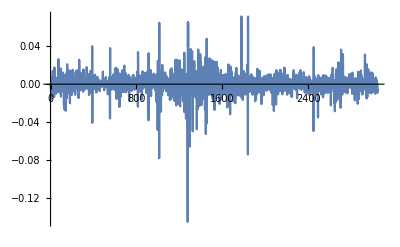

```mathematica
ListLinePlot[rsWethUsdc90dFiltered30MinCandle, PlotRange->All]
```

```mathematica
edistWethUsdc90dFiltered30MinCandle = EstimatedDistribution[rsWethUsdc90dFiltered30MinCandle, StableDistribution[1, aWU90dC30m, bWU90dC30m, locWU90dC30m, scaleWU90dC30m]]
```

StableDistribution[1,1.55263,-0.0735773,-0.0000556332,0.00439438]

```mathematica
rsWethUsdc90dFiltered1HourCandle = Differences[Log[twapsWethUsdc90dFiltered1HourCandle]]
```

{-0.0012941,-0.00939344,-0.0241963,-0.0104817,-0.0147229,0.00820584,0.014547,0.00112845,-0.0193036,0.0015467,0.0227744,0.00588498,0.0156569,-0.00128477,0.00383628,0.00765843,-0.0210875,0.0282886,0.0179942,0.00895628,0.0123902,0.00146154,0.00885738,-0.00492522,0.00591001,-0.0150075,0.00572474,-0.00151273,-0.00691957,0.000305489,0.00603401,-0.0100807,0.000682628,0.00289066,-0.0146574,0.0102704,0.0344637,0.00778817,0.0186024,0.00506249,-0.00892867,-0.00431243,0.00701086,-0.0161606,-0.00113936,-0.012692,0.000360494,0.0312663,-0.0188007,0.00704985,0.010712,0.0109927,0.00574422,-0.00522957,-0.00581162,0.0174255,0.0193901,0.0145689,-0.00244056,0.00546382,0.00668475,0.00364873,-0.0249162,-0.011591,-0.0228768,-0.0253583,0.00692255,0.00215623,-0.0106241,-0.0478116,-0.0183125,0.00791559,-0.0236331,-0.00521017,-0.00563152,-0.00177441,0.0111625,0.0321856,0.00678772,-0.0188758,0.00455526,0.0139082,0.0189708,-0.0114339,0.0166378,0.00651145,-0.00655183,-0.0117856,0.00907496,-0.0115368,-0.0149498,-0.00193373,0.0155644,0.0014861,0.00242527,-0.0157198,0.00129305,-0.00477816,-0.017937,-0.0152772,0.00743036,0.00291753,-0.00947762,0.0187403,-0.00177333,0.0103974,0.00629432,-0.0000214817,0.00563643,-0.0111222,-0.0124043,-0.00699624,0.00972473,-0.00190175,-0.0202832,0.00107855,0.00241894,-0.00819129,0.00840919,0.00967682,0.022379,0.00234826,0.0144718,0.0013018,0.0111105,0.000332482,-0.000134127,-0.0102255,-0.00747374,-0.0100704,-0.0290967,0.0216257,0.0169805,0.0462855,0.0155823,0.00060125,0.00484828,-0.00178179,0.00678203,-0.00217996,-0.00778384,-0.00111525,0.0178142,0.0111511,-0.00443252,-0.00200192,-0.00437384,0.000538142,0.00743398,-0.0025352,-0.00431194,-0.0106806,0.0113255,0.00980401,0.00225378,-0.0040591,0.00357938,-0.00524702,-0.00368089,0.0102967,0.0115506,-0.000148314,-0.00216172,0.00130508,-0.000413909,0.00828751,-0.0031985,0.00176965,0.0259262,0.00826952,-0.00689629,-0.000758883,-0.0049228,0.00453319,0.000734732,-0.00383704,0.0191525,0.00630641,-0.00544079,-0.0157458,-0.0000538651,-0.013288,-0.00261155,0.00789323,-0.00689467,0.00818365,0.0234902,0.0130463,-0.00754792,0.00245135,-0.00598091,0.0106099,0.00386107,0.0396993,-0.0452123,0.00766826,-0.00403656,0.00603463,-0.00466538,-0.00261885,-0.00127849,-0.0101564,0.00372127,0.00926992,0.00267257,-0.00477485,0.0167269,0.000933011,0.000192249,0.00685637,-0.00820991,0.00507312,-0.00432025,-0.0110354,-0.00698569,0.00250417,-0.00504121,0.00877336,0.0102957,-0.00281021,-0.00562736,0.0014454,-0.000400875,0.00569195,0.0028523,0.00599179,-0.00135385,0.001688,-0.00510824,-0.00174067,-0.00699027,0.000740825,0.00267789,-0.002698,0.00236155,0.00446606,0.000211853,0.00457926,-0.00472001,-0.00303777,-0.00106019,0.00611192,-0.00101119,0.0221515,0.00269457,0.00191348,0.00686818,-0.00212883,-0.0000333065,-0.00590221,-0.000872327,0.00443358,0.00618739,0.000978685,-0.00137111,-0.0044582,0.0121537,0.012713,0.00281359,-0.00333111,0.00492416,-0.00217514,0.00410975,-0.00148692,-0.000771305,0.00484947,-0.013151,0.00154328,0.000245555,-0.00789836,-0.00759518,0.00433302,0.0104016,0.00181102,0.00161976,-0.00315996,-0.0351516,0.040803,0.000546262,0.00344737,0.0094448,-0.00133529,0.00172134,-0.010834,0.00855037,0.00834883,0.00846601,0.00723202,0.00469582,0.00866432,0.00337486,0.0137537,0.0143363,-0.00356706,-0.00568652,0.00479291,-0.00924879,-0.00506178,0.0161896,0.00296944,0.0274497,0.0125781,-0.00409099,-0.00385356,0.00556396,0.0256687,0.00661141,-0.0292281,-0.0097714,-0.0121292,0.0112151,0.0245253,0.00573675,-0.00730707,-0.0144401,0.0148419,0.0156641,0.0142715,0.0035959,-0.00952215,-0.0355128,-0.018082,0.0161683,0.0166066,0.0108901,-0.00637733,-0.0220459,-0.00396726,0.00237482,0.017944,-0.0103872,-0.00866101,-0.00940875,-0.0026819,0.00568391,0.0228077,0.00280706,0.00265709,-0.00284089,0.00308071,-0.00696032,-0.00304267,0.00569525,0.0192498,-0.00288628,0.0126126,-0.00040282,-0.00271909,0.0212392,-0.00410335,-0.0098011,0.00538715,-0.00559571,0.00228718,-0.00763678,-0.00945856,0.00588384,0.00175553,0.00902914,0.0057251,0.000756119,-0.00426355,0.00958883,0.0160935,0.000343066,-0.0196071,-0.0136214,0.00194127,0.0133585,0.00178386,-0.00367229,-0.00526729,-0.0103905,-0.00592555,-0.0111679,0.00562247,0.00843029,0.00384391,-0.00631954,0.00711197,0.0000715682,-0.0018841,0.0124739,0.00168979,0.00267713,0.0150261,-0.00165389,-0.00858756,-0.00185717,-0.00396376,-0.00542598,-0.0101666,0.00963832,0.0123639,0.0037379,-0.00233891,0.0105406,-0.00628502,-0.00515027,0.000879561,0.00949945,-0.00138879,-0.00474051,0.000717644,0.0100192,0.020237,-0.0207963,0.052254,0.0130797,0.00232995,-0.0022154,0.0110306,0.0111614,-0.00767684,-0.00335574,0.00415127,0.00346162,-0.000483502,0.00326224,0.00668189,0.00668463,-0.00201467,-0.00880873,-0.00675781,0.00155063,-0.028712,0.00572009,0.00688331,0.0153514,0.00813714,-0.00248631,-0.006763,-0.000375609,0.00737534,-0.00385056,0.0019901,0.000198811,0.00510032,0.0116912,0.0188459,0.0134263,0.00366521,-0.0000202228,-0.00434395,0.00492858,-0.0108023,-0.00670333,0.018204,-0.000340032,-0.0104199,0.0218255,-0.0010619,-0.00754958,-0.012836,-0.0487143,0.028263,-0.00545802,-0.00530323,-0.018157,-0.00673611,-0.00679897,0.017294,-0.00188778,0.013879,-0.00355901,0.00637078,0.022872,-0.0133469,-0.0113365,0.00262367,0.00972989,0.0100581,-0.0018835,0.00807372,-0.000664149,0.0169381,-0.00386746,0.00511166,0.00789178,0.0026353,0.0192524,0.0135869,-0.0000334813,0.00175676,-0.00480754,-0.00364428,-0.00087381,-0.00858292,0.00584471,0.00225291,0.0103889,-0.0291231,-0.0156554,-0.00598179,-0.0289033,0.0182389,0.00843401,-0.00189759,-0.0486656,0.00656987,0.0150269,-0.00573566,-0.00699279,0.00348541,0.0114188,-0.0766094,0.0495032,-0.034843,-0.0224625,0.024264,0.0140562,0.0153153,-0.0227438,-0.0117354,-0.0212833,-0.00807792,0.0121961,0.016902,-0.0029743,-0.0187685,0.0345767,0.0192089,-0.0143146,-0.00200294,-0.00243474,0.0114072,0.000437347,0.0119957,0.0175754,0.00207719,0.0121896,-0.00628157,0.0115755,0.0183623,0.0071341,-0.00367281,-0.00846574,-0.00714214,-0.0132724,0.00961144,0.0102557,-0.00102612,0.00126949,0.0000786298,-0.0108557,-0.00365595,-0.00285802,-0.0177863,-0.00735803,-0.00228951,-0.0161318,0.0086849,0.00837138,-0.00626809,0.00255444,-0.0226809,-0.0157427,0.000574938,-0.0089521,0.0216996,0.00161998,-0.0215092,0.00525226,0.0196051,0.00162947,-0.00505536,0.00102626,0.00228188,0.00799437,-0.00959126,-0.000373717,0.00650619,-0.00530254,-0.0203736,-0.00673919,-0.0106307,-0.00825197,-0.0283604,0.0138139,-0.0336105,-0.0165539,-0.00108657,0.0363906,0.00522162,-0.012247,-0.0279668,-0.011188,-0.0392792,0.0140206,0.0248475,0.0245239,0.0192418,-0.00573792,-0.0103429,0.0123291,-0.0138041,-0.0169138,-0.0184294,-0.024684,-0.0204641,0.0455715,0.00947227,0.0104339,-0.0379973,-0.0128265,0.0264401,0.0143223,-0.000668989,0.00541914,0.0272934,0.0125127,-0.0132218,0.00480567,-0.0121086,0.00699344,0.00849575,-0.0214613,-0.0243592,-0.0104821,0.0124331,0.0154605,-0.0161291,0.00399398,0.0153613,-0.00573467,-0.0114158,0.00803497,-0.0299383,-0.0348267,-0.0234018,-0.0415037,-0.0173636,0.011688,-0.00286386,0.00392249,-0.00813305,-0.0471791,-0.0499205,-0.214646,0.0919721,0.104027,0.0650292,-0.0185358,-0.0492683,0.00774173,-0.0460781,0.0524762,-0.0379616,-0.0963281,0.00422759,0.0494469,0.0260708,0.0376831,0.0104027,0.0338998,-0.021013,-0.00332139,0.01251,0.040997,0.0436868,-0.0053785,-0.0279027,-0.0510988,0.0240177,0.0118012,-0.00254107,0.00992314,-0.0105293,0.00703635,0.035696,-0.0147688,-0.0226959,-0.01217,-0.00813089,-0.00256247,-0.0211896,0.0202049,0.00410991,-0.0235389,-0.00232114,0.00806105,-0.0708791,-0.0258258,0.0048203,-0.00910545,-0.0214291,-0.0437344,0.0135306,0.0344801,0.00460629,0.0128563,0.0057863,-0.0365698,-0.0351768,-0.0316194,0.00220857,0.0172454,0.0350072,0.00549788,0.0367225,-0.00607989,0.00453372,-0.0209481,-0.0183107,0.00915097,-0.0292831,-0.000930007,0.00429248,0.0232195,-0.00296,-0.00318207,-0.0158749,0.0247332,-0.021289,0.000367848,-0.0147724,-0.020053,-0.0147157,-0.0291446,-0.0479736,0.0163756,0.0263655,-0.0368352,-0.06705,0.0206743,-0.0197836,-0.0485451,0.0407481,0.00476796,0.0439972,0.0477376,0.00724105,-0.0115687,0.0326188,-0.0176598,0.00578556,0.0148619,-0.0177211,-0.0011764,0.0370896,0.036244,-0.00502727,-0.00928528,0.0330669,0.03636,-0.000794619,0.0200143,0.000775624,0.0140905,0.0272715,0.0137846,0.00845554,-0.00979266,-0.00047401,0.0413373,-0.0110942,-0.0290495,-0.0077595,-0.000493834,0.0186925,0.011148,-0.00858051,-0.0238053,-0.0400413,-0.0107169,-0.0010372,0.0434581,0.0216406,-0.00891953,-0.00538814,0.00949722,-0.0167082,-0.000775799,0.0277059,0.0305213,-0.00536035,0.00837233,0.0325365,0.00744402,-0.00663069,0.00509895,0.0206239,-0.00414016,-0.00369765,-0.0173349,0.0110792,-0.0129434,-0.0182479,-0.00515184,-0.0029229,-0.0047764,0.00572359,0.00681618,0.0175886,0.00939277,0.0120975,-0.0174053,-0.0306361,-0.0131389,-0.00500391,0.00414471,0.0148534,0.0060136,0.00300095,0.013594,0.00160629,0.00906468,-0.00317154,0.0137047,-0.00813121,-0.0142553,-0.00152433,0.00109081,-0.0113489,-0.00768726,0.0154724,-0.00688117,-0.0120338,-0.00927645,0.00904654,-0.00194751,-0.0151355,-0.0211195,-0.0256399,0.00274905,-0.0289856,0.00311602,-0.00484641,0.0188107,0.0240086,-0.01353,-0.00600392,-0.0178883,0.00041605,0.00735817,-0.0161636,-0.0455257,0.00873186,0.0188407,0.0321121,0.00133565,0.00256067,-0.00364937,0.0142829,-0.0036941,-0.0170464,-0.0201625,-0.00710644,-0.00288611,0.00284228,-0.0230984,0.00433128,-0.0275039,0.0115466,-0.0319235,-0.00771588,-0.00844404,0.00730837,0.00638166,0.00925695,-0.0312138,0.0026566,0.0245846,0.0044872,0.0166774,0.0285583,0.0156512,0.00328341,-0.00500426,-0.00644106,0.00348683,-0.00596326,-0.00774951,-0.0123055,0.00964994,0.0141724,0.0106783,0.00466503,-0.00418728,-0.00407016,-0.0118364,-0.00637561,-0.0176246,-0.0184907,0.000268613,-0.00127051,0.00865545,0.0164549,0.089497,0.0423522,-0.0208488,2.12254×10^-6,0.0053921,0.0132907,-0.0124978,-0.0225969,-0.00816368,0.0101791,0.00440036,-0.018623,0.0234938,-0.020197,-0.00305135,-0.00710412,0.00858124,-0.00790235,0.00936683,0.00833752,0.00302318,0.0046938,-0.0171702,0.0142753,0.00676129,0.00208907,0.00116304,0.0052074,0.016854,0.00298927,-0.00299108,-0.00278577,0.00832414,0.00609375,0.0115385,0.011892,-0.00795538,0.0000639027,-0.000167785,-0.0050155,-0.00898109,-0.00827721,0.00284233,-0.0033578,-0.00527723,0.00754765,0.017464,0.0179267,0.0106031,-0.00252356,0.00677932,0.0133633,-0.0185224,-0.00346057,-0.010544,-0.000770574,0.00092748,0.013321,-0.00180188,-0.0111563,0.00177417,0.0101783,0.00248479,0.00551513,-0.0217116,-0.0238835,0.0087551,-0.000164684,-0.0264604,-0.0163268,-0.0023619,0.00124636,0.00794775,-0.00562918,-0.0134513,0.0201362,-0.00701217,0.0087424,0.00377169,0.0111149,0.00102107,-0.00436573,0.0119223,0.00170911,-0.0141093,0.0196286,0.00901403,-0.00188142,0.0023976,0.00356037,-0.00246373,0.0055925,0.00277649,-0.000521804,-0.029022,-0.0196281,-0.0074488,-0.00516444,-0.00697616,0.0127463,-0.00540212,0.000105092,-0.000996741,0.000947258,-0.0220139,0.00555942,0.0141572,0.0108638,0.012686,-0.00311328,0.00234005,0.000526961,-0.00682497,0.0103438,0.0120844,-0.0013824,-0.00490355,-0.0021672,-0.0114053,0.00858744,0.0103122,-0.00173041,-0.0097833,-0.00242831,-0.000637409,0.00877699,-0.00661491,0.00785111,0.0165937,0.0112232,0.00119587,-0.00423626,-0.000676788,0.000379677,-0.00691273,0.000358558,0.0124191,0.0117715,-0.00437439,0.00298034,-0.0154748,-0.000468342,-0.00389883,-0.0153326,-0.00978585,0.00777336,-0.0266987,-0.0118,-0.00126481,-0.00889627,0.00484177,-0.0158411,-0.0327195,0.0104915,-0.00744525,-0.000632951,0.0159287,-0.00309067,-0.00571841,0.00117362,0.00538867,-0.0173576,-0.0379915,-0.00591382,0.0147172,0.00804599,0.01915,0.0113871,0.0111423,-0.0115324,0.00952897,-0.0201143,-0.00961352,-0.00036019,-0.00174056,0.00804524,0.0139242,0.011378,-0.0131077,-0.0000160461,0.00421173,0.0171157,-0.00359611,-0.00450502,0.0100182,0.0161194,-0.00038198,-0.0080995,-0.00325895,0.0032708,0.0187834,-0.0177846,0.0047134,-0.00175758,-0.00215127,-0.002971,-0.0101417,-0.00356038,0.00407345,-0.0046887,0.00180119,0.0208902,-0.0095054,-0.00642249,-0.00569552,-0.00644413,-0.0109336,-0.00971393,-0.000142314,-0.00206448,-0.00499903,0.0111543,0.00523848,-0.00724996,-0.0212392,-0.000328258,0.0165968,0.00478763,-0.000135959,-0.0144011,0.00521025,0.00303424,0.00504557,0.00101508,-0.00530451,0.00465818,-0.00600279,-0.0149278,-0.0145622,0.00621787,0.0043072,-0.00398839,-0.0197602,0.00455476,-0.00817934,-0.00175919,-0.0218371,-0.00129088,0.00380165,-0.00276214,0.00160008,0.0102873,-0.000637267,0.00245463,0.0277299,0.00871102,0.0130382,-0.00762243,-0.00411295,-0.00806793,0.000724258,0.00890668,0.0024938,-0.0017114,-0.00420394,-0.00767731,-0.00283168,0.000116806,0.0109929,-0.00999281,-0.0198979,-0.0018207,-0.004514,0.00696894,0.00263064,0.00469954,0.0061506,-0.00027183,-0.00254488,-0.0023037,-0.00673069,0.00832445,0.0166375,0.012955,0.00133117,0.0204564,0.0184066,-0.00762892,-0.00361871,-0.000792056,0.000915494,-0.0050559,-0.00387898,0.00533813,0.00161225,0.000383698,-0.00680211,-0.00227587,0.00517242,-0.00301902,0.0137127,0.0192007,-0.00261384,0.0098416,-0.00418281,-0.00649396,-0.00881918,0.00525002,0.0062008,0.000847117,0.0105118,0.00212531,-0.00584622,0.00375379,0.00790757,0.00296729,-0.0000764963,-0.00271195,-0.0109511,0.000704812,-0.00167003,0.00222784,0.00217801,-0.0129713,-0.00677012,0.00435604,0.0105383,-0.000958673,-0.0198356,-0.000219197,0.00543539,0.00542252,-0.0110759,-0.00457577,0.00394839,-0.00247434,0.00338092,0.000203,0.00309958,0.0012171,-0.0051046,-0.00532081,-0.018683,-0.00681364,0.00306327,-0.0101975,-0.00179384,-0.0103758,0.00326322,0.00528367,-0.00801237,0.000974888,-0.0150801,0.00572861,0.00801428,0.00720188,0.00488335,-0.0038248,0.00304976,0.008319,-0.003844,-0.000822836,-0.000341455,-0.0122885,-0.010619,0.00328207,0.00571093,-0.0383092,0.00206379,0.00986234,-0.00021928,-0.000416232,0.000495876,0.0116051,-0.00114484,-0.0125009,-0.00100441,0.00348239,0.00568923,-0.00638835,-0.00304277,0.00627256,-0.00804012,-0.00847842,0.00527838,-0.0145063,-0.00815206,-0.00955673,-0.0113306,0.00273622,-0.0147734,-0.0178795,0.0121509,0.00866658,0.002415,0.00570551,0.0102709,0.00162146,-0.0140716,-0.0130787,0.00989884,0.0130122,-0.00343047,0.00571281,-0.000135609,-0.00639472,0.00344081,0.00400718,-0.0060211,0.00745442,-0.00343697,-0.00171008,-0.013836,0.00134676,0.00332667,0.00249885,-0.0159085,-0.00496909,-0.00733892,0.00896781,-0.00346551,0.00697238,0.00969443,0.000614359,-0.00351155,-0.00262461,-0.00790318,-0.0290954,-0.0159504,-0.00936422,0.010574,0.00720206,0.00781923,0.00411121,0.00422791,0.0193097,0.0295205,0.0069152,-0.00207255,-0.00397921,-0.00675426,-0.00784839,-0.0117904,-0.0186685,-0.0206979,0.00559483,-0.0452594,-0.0010944,-0.00594529,-0.014065,-0.0193764,0.00814122,0.0119351,0.0106061,-0.014344,-0.0194366,0.000392771,0.00115321,0.00254537,-0.0213141,-0.00774783,0.0010795,0.0242412,0.00756068,0.00972191,-0.000957534,-0.00956901,-0.0022591,-0.00241011,-0.0296387,-0.00680816,0.0109481,-0.0264686,-0.0365919,-0.00945587,0.0609892,0.0177554,0.00230833,0.00833756,-0.00480724,-0.0055726,-0.0105714,-0.00944353,0.03484,0.0336373,0.00603512,0.00072387,0.00130216,0.00372819,-0.00523813,-0.0106538,0.00301437,0.00365843,0.000404859,0.00548513,-0.0101902,-0.00418997,0.000906365,-0.0120625,-0.00622167,-0.00935106,0.00463923,0.00322816,0.00808523,-0.00803339,-0.0186717,-0.0064605,0.00310783,0.00286737,0.00662379,0.00419559,0.000083875,0.00737759,-0.00348675,0.0125808,0.00331526,-0.00209701,0.0123044,0.000232928,0.0157637,-0.000590066,-0.00301766,-0.00455768,-0.0041327,-0.0072383,0.00646061,-0.00753522,0.00951817,-0.00137874,-0.00511877,-0.00798561,-0.00397857,-0.0127422,-0.00381603,-0.00905081,-0.0200314,-0.00725568,-0.00620233,0.00283735,-0.0194601,-0.00252828,0.00134175,0.0128666,0.00482291,0.00206355,-0.00714427,-0.0139373,0.00450107,-0.0051638,0.00372823,0.00907861,-0.00421693,-0.0358477,-0.0202306,0.0154573,0.00629004,0.0162906,-0.00386356,-0.0252872,0.015652,-0.0121158,0.00631525,0.0135046,-0.00181622,-0.0113363,0.00306231,0.0101013,0.0202928,0.0106909,0.0177692,0.00459609,-0.00705124,-0.00600908,0.00332132,-0.0146672,-0.00887911,0.00689624,0.0099005,-0.00781295,-0.00185977,0.00283063,-0.00792733,-0.00574474,-0.000458045,0.00459319,0.00116538,0.0610492,0.0132503,0.00885643,-0.00814342,0.00331463,-0.000853562,0.000575169,0.022219,-0.000594212,0.0203352,-0.00409039,-0.0250254,-0.000313955,0.00619466,0.0028855,0.0266109,0.0185151,-0.00735743,-0.00385612,0.0166255,0.00333954,-0.0103708,-0.0127511,0.0120388,0.00851822,-0.00747829,-0.0010489,0.00688954,-0.00481085,0.0221793,-0.0123116,0.00736885,0.00545394,0.010248,-0.00149937,0.0146894,0.00636515,-0.00309933,0.0041733,0.000818091,-0.00416369,0.000715836,-0.00952928,-0.00844322,-0.0065269,0.00283923,-0.00539034,-0.00282712,-0.0124691,-0.0104712,0.0138421,0.00717897,-0.0038457,-0.00942509,0.00704325,0.00803376,-0.0100288,0.000751933,-0.014457}

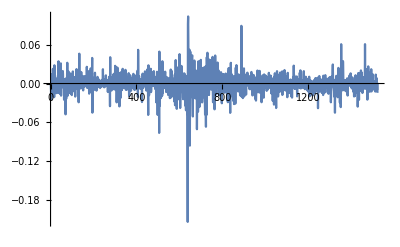

```mathematica
ListLinePlot[rsWethUsdc90dFiltered1HourCandle, PlotRange->All]
```

```mathematica
edistWethUsdc90dFiltered1HourCandle = EstimatedDistribution[rsWethUsdc90dFiltered1HourCandle, StableDistribution[1, aWU90dC1h, bWU90dC1h, locWU90dC1h, scaleWU90dC1h]]
```

StableDistribution[1,1.59768,-0.0971292,-0.000157254,0.00790013]

```mathematica
rsWethUsdc90dFiltered2HourCandle = Differences[Log[twapsWethUsdc90dFiltered2HourCandle]]
```

{-0.0106875,-0.034678,-0.00651707,0.0156755,-0.0177569,0.0286594,0.0143721,0.0114947,0.0072011,0.0269505,0.0138518,0.00393216,-0.00909746,0.00421202,-0.00661409,-0.00404668,0.00357329,-0.00438701,0.0422518,0.0236649,-0.0132411,-0.00914979,-0.0138314,0.0316268,-0.0117508,0.0217047,0.000514654,0.0116139,0.0339591,0.00302326,0.0103335,-0.0365072,-0.0482351,0.00907878,-0.0584357,-0.0103969,-0.0288432,-0.00740593,0.0433481,-0.0120881,0.0184635,0.00753693,0.0231493,-0.0183374,-0.00246185,-0.0168835,0.0170505,-0.0132945,-0.00348511,-0.0332141,0.0103479,0.00926271,0.00862407,0.00627283,-0.0054858,-0.0194005,0.00782298,-0.0192047,-0.00577235,0.018086,0.0247272,0.0157736,0.011443,-0.0103597,-0.0175441,-0.00747108,0.063266,0.0161836,0.00306649,0.00460207,-0.00889908,0.0289653,-0.00643444,-0.0038357,0.00489878,-0.0149925,0.0211295,-0.00180531,-0.00166764,0.00661579,0.0114023,-0.000856642,0.0078736,-0.00142885,0.0341957,-0.00765517,-0.000389611,-0.00310231,0.0254589,-0.0211866,-0.0133419,0.00528169,0.00128897,0.0365366,-0.00509656,0.00462901,0.0435603,-0.0375441,0.00199807,-0.00728424,-0.0114349,0.0129912,-0.00210228,0.0176599,0.00704862,-0.00313679,-0.0153556,-0.00448151,0.00373214,0.00748546,-0.00418196,0.00529108,0.00884409,0.000334143,-0.00684891,-0.00624944,-0.0000201069,0.00682761,0.00479112,-0.00775779,0.00505173,0.0211403,0.00460805,0.00473935,-0.00593552,0.00356125,0.00716608,-0.00582932,0.0248667,-0.000517517,0.00274902,0.00262283,0.00407817,-0.0116077,-0.0076528,-0.00326216,0.0122127,-0.0015402,0.00565139,0.00399363,0.00810952,-0.00911264,0.0168992,0.015698,0.0133601,0.0171285,0.0107692,-0.000893609,-0.0143106,0.019159,0.0400277,-0.00794455,0.0312326,-0.0226167,-0.0219006,0.0357404,-0.00157032,0.000401805,0.0299355,-0.00592625,-0.0535948,0.0327749,0.00451278,-0.0260132,0.0203188,-0.0190482,-0.0120907,0.0284916,0.00546415,0.000239813,-0.010003,0.024945,0.00972631,-0.00312191,0.0171359,-0.00441395,-0.00330853,-0.0170953,0.00763937,0.0147542,-0.00350743,0.0256824,-0.0192641,-0.0116801,0.0151424,-0.00893958,-0.016316,-0.00554545,0.0122742,0.000792427,-0.00181253,0.0141637,0.0177032,-0.0102415,-0.00582093,-0.0155926,0.0220022,0.00139898,0.00425554,-0.0042707,0.00811066,-0.00402287,0.0302562,0.0314577,0.0154097,0.00881519,0.00348451,0.000795527,0.00297812,0.00994413,0.00466996,-0.0155665,-0.0271613,0.0126034,0.0234886,-0.00924931,0.00699973,-0.00186046,0.00529913,0.0305371,0.0170915,-0.00436417,-0.00587376,0.0115007,-0.0107599,0.0207636,-0.0203855,-0.0204513,-0.0107613,-0.0248932,0.0104951,0.0119912,0.00281177,0.00952505,-0.00871283,0.019788,0.00619023,0.016274,0.0012442,0.0105271,0.0328394,0.00172327,-0.00845183,-0.00945673,0.00809761,-0.0187343,-0.0216372,-0.0106644,0.00653642,-0.0420957,0.00929128,-0.00350738,-0.0651905,0.0146602,0.0018015,0.0293716,-0.0344792,-0.0293612,0.0290981,-0.0217428,0.0537856,-0.0163175,0.00897246,0.0124331,0.0196526,0.00590803,0.0299378,0.00346129,-0.0156079,-0.00366098,0.00922962,0.00134812,-0.0145117,-0.0206443,-0.00964754,-0.00744694,0.00210329,-0.0201265,-0.0151678,0.0127475,-0.0198892,0.0248573,-0.0034259,0.00330814,-0.00159689,0.00613248,-0.0256762,-0.0173699,-0.0366124,-0.0197966,-0.0176405,0.0416123,-0.0402137,-0.0504672,0.0388682,0.0437658,-0.0160808,-0.00147506,-0.0353432,-0.0451481,0.0550438,-0.0275635,0.0136137,0.0136533,0.0327126,-0.000709175,-0.00730295,0.0154892,-0.0458204,0.00195093,-0.0006686,0.0193553,-0.0171504,-0.0219034,-0.0582285,-0.0588673,0.00882412,-0.00421056,-0.0970996,-0.122674,0.169056,-0.067804,-0.0383363,0.0145146,-0.0921005,0.0755177,0.0480859,0.0128868,0.00918865,0.0846838,-0.0332812,-0.0270811,0.0092601,-0.000606139,0.0427323,-0.0374647,-0.0203009,-0.023752,0.0243148,-0.0258601,-0.0628181,-0.0210055,-0.0305345,-0.0302038,0.0390864,0.0186426,-0.0717466,-0.0294108,0.0522526,0.0422204,-0.00154618,-0.0392588,-0.0201321,0.00336247,0.0202595,-0.019057,0.0034442,-0.0144046,-0.0347688,-0.0771182,0.0427411,-0.103885,0.000890749,-0.00779703,0.0487652,0.0549786,0.0210501,-0.0118742,-0.00285915,0.0359132,0.0312167,0.0237816,0.0355654,0.0207899,0.041362,0.0222401,-0.0102667,0.0302431,-0.036809,0.0181987,0.00256745,-0.0638465,-0.0117541,0.0650987,-0.0143077,-0.00721094,0.0269301,0.025161,0.0409088,0.000813332,0.0257229,-0.00783781,-0.00625571,-0.0311913,-0.00807473,0.000947191,0.0244048,0.0214903,-0.0480414,-0.0181429,0.0189981,0.00901456,0.0152003,0.00589314,0.00557351,-0.0157796,-0.0102581,0.00778511,-0.018915,-0.00022991,-0.017083,-0.0467594,-0.0262366,-0.00173039,0.0428193,-0.0195339,-0.0174723,-0.00880538,-0.0367939,0.0509528,0.00389631,0.0106335,-0.0207405,-0.0272689,-0.0000438292,-0.0187671,-0.0159573,-0.0396394,-0.00113567,0.0156386,-0.0285572,0.0290718,0.0452357,0.0189346,-0.0114453,-0.00247643,-0.020055,0.0238223,0.0153433,-0.00825744,-0.018212,-0.0361153,-0.00100189,0.0251103,0.131849,-0.0208467,0.0186828,-0.0350947,0.00201542,-0.0142226,0.00329679,-0.0101555,0.00067889,0.0177043,0.00771698,-0.00289496,0.00885035,0.00637044,0.0198432,-0.00577685,0.0144179,0.0234305,-0.00789148,-0.00518329,-0.0172583,-0.000515472,0.00227042,0.0353907,0.00807954,0.0201426,-0.0219829,-0.0113146,0.0142485,-0.0129582,0.0119525,0.00799992,-0.0455951,0.00859042,-0.0427872,-0.00111554,0.00231857,0.00668484,0.00173023,0.0148866,-0.00334466,0.0136314,0.00551922,0.00713261,0.00595798,0.00312877,0.00225469,-0.0486501,-0.0126132,0.0057701,-0.00529703,-0.0000494827,-0.0164545,0.025021,0.00957274,0.00286701,0.00351887,0.010702,-0.00707075,-0.00281788,0.00858184,-0.0122116,0.00813958,0.00123621,0.0278169,-0.00304039,-0.000297111,-0.00655417,0.0241906,-0.00139405,-0.0159432,-0.0192315,-0.00201249,-0.0384987,-0.0101611,-0.0109994,-0.022228,-0.0080782,0.012838,-0.00454479,-0.0119689,-0.0439053,0.0227632,0.0305371,-0.000390172,-0.0105854,-0.00997371,0.00630468,0.0253023,-0.0131237,0.0213275,-0.00810113,0.0261376,-0.00848148,0.000011847,0.000998885,0.00295583,-0.00512227,-0.0137021,-0.000615252,0.0226914,-0.0159279,-0.0121397,-0.0206475,-0.00220679,0.00615523,-0.00201148,-0.0215675,0.0213844,-0.0145371,0.00824448,0.00606066,-0.00064633,-0.0209306,-0.00834435,0.000318811,-0.0152054,-0.00993853,-0.023128,0.00103951,0.0118874,0.00181736,0.036441,0.00541581,-0.0121809,0.00963094,0.0007824,-0.0118813,-0.00271487,0.00100008,-0.0217186,0.00245494,0.00733018,0.00587877,-0.00484858,0.00159376,0.0295925,0.0217876,0.0107777,-0.00441077,-0.00414041,0.00145915,0.00199594,-0.00907798,0.0021534,0.0329134,0.00722776,-0.0106768,-0.00356916,0.00704791,0.0126371,-0.00209243,0.0108749,-0.00278845,-0.0102463,0.000557812,-0.0107933,-0.00241408,0.00957966,-0.0200548,0.0108579,-0.0156517,0.00147405,0.00358392,0.00431668,-0.0104254,-0.0254967,-0.00713422,-0.0121696,0.00854689,-0.00703748,-0.00935144,0.0152162,0.00105855,0.0113688,-0.00466684,-0.01263,-0.00733689,-0.0325983,0.0119261,-0.000635511,0.012101,-0.0136457,0.00247797,-0.000699114,0.00322979,-0.0165185,-0.00922788,-0.0177088,-0.00859443,-0.0326529,0.0208175,0.00812051,0.0118924,-0.0271504,0.022911,0.00228235,-0.00653033,0.00744799,0.00143332,-0.00514706,-0.0124893,0.00582552,-0.0208776,0.00162889,0.00350687,0.0103088,-0.00613616,-0.0369986,-0.0253146,0.0177761,0.0119304,0.0235376,0.0364357,-0.00605177,-0.0146027,-0.030459,-0.015103,-0.0463538,-0.0200103,-0.0112352,0.0225412,-0.0337805,0.00154598,-0.0187688,-0.00666833,0.0318018,0.00876438,-0.0118281,-0.0320488,0.00413989,-0.0630605,0.0515333,0.0200637,0.00353032,-0.016144,0.0253965,0.0396724,0.00202603,-0.00150994,-0.0076394,0.00406329,-0.00470508,-0.00328361,-0.0182842,-0.00471182,0.0113134,-0.0267051,-0.00335267,0.00949116,0.00427946,0.00389084,0.015896,0.0102074,0.0159966,-0.00360773,-0.00869038,-0.000777691,0.00198295,-0.00649751,-0.0119642,-0.0165582,-0.0290822,-0.013458,-0.0166228,-0.00118653,0.0176896,-0.00508072,-0.00943624,-0.00143557,0.00486169,-0.0560783,0.0217473,0.0124271,-0.00963521,-0.00580053,0.0116883,-0.00827403,0.0303941,0.0284601,-0.00245515,-0.00268777,-0.0235463,0.0167967,-0.00967272,-0.00509671,-0.00620278,0.00575856,0.0742995,0.00071301,0.00246107,0.0227942,0.019741,-0.0291158,0.0058807,0.0294964,0.0111577,0.0127693,-0.00703131,-0.00071229,0.00103993,0.00584064,0.0173685,-0.00494273,0.0157019,0.0131901,0.00326582,0.00499139,-0.00344785,-0.0179725,-0.00368767,-0.00821746,-0.0229403,0.0210211,-0.0132708,0.015077,-0.00927689}

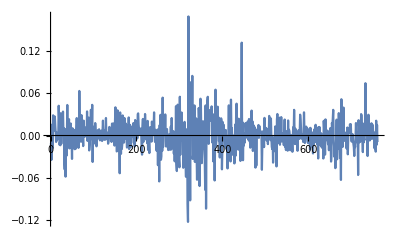

```mathematica
ListLinePlot[rsWethUsdc90dFiltered2HourCandle, PlotRange->All]
```

```mathematica
edistWethUsdc90dFiltered2HourCandle = EstimatedDistribution[rsWethUsdc90dFiltered2HourCandle, StableDistribution[1, aWU90dC2h, bWU90dC2h, locWU90dC2h, scaleWU90dC2h]]
```

StableDistribution[1,1.66239,-0.0643151,-0.000079592,0.0126146]

```mathematica
0.007900125269736371 * (2^(1/1.6))
```

0.0121837

```mathematica
(* :) ... 1h -> 2h looks way more stationary *)
```

```mathematica
rsWethUsdc90dFiltered4HourCandle = Differences[Log[twapsWethUsdc90dFiltered4HourCandle]]
```

{-0.0453655,0.00915841,0.0109024,0.0258668,0.0341516,0.0177839,-0.00488545,-0.0106608,-0.000813724,0.0659167,-0.0223909,0.0177954,0.0099539,0.0121285,0.0369823,-0.0261737,-0.0391563,-0.0688326,-0.0362492,0.03126,0.0260004,0.00481185,-0.0193454,0.00375603,-0.0366993,0.0196106,0.0148969,-0.0248863,-0.0113817,0.0123137,0.0405008,0.00108329,-0.0250152,0.0794496,0.00766856,0.0200662,-0.0102701,-0.0100937,0.0193242,0.00494815,0.0105456,0.00644475,0.0265405,-0.00349192,0.00427232,-0.0080602,0.0378255,-0.000467552,0.00601625,-0.00528617,0.00155629,0.0155576,0.00391183,-0.0198372,0.0112176,0.00110912,0.00917823,-0.0130984,0.0068075,-0.00296667,0.026192,0.00934741,-0.00237426,0.00133676,0.0243492,0.00537184,-0.00752954,-0.010915,0.0106724,0.00964502,-0.00100313,0.0325972,0.0304887,0.00987559,0.00484846,0.0320832,0.00861593,0.0138398,-0.00116852,0.0240093,-0.0208199,-0.0215004,0.00127058,0.016401,0.00570396,0.014942,0.00660441,0.0127219,-0.0204039,0.0223936,0.0221749,-0.0309442,0.0062028,-0.0218615,0.0130666,0.0123511,0.00746174,-0.0214135,0.0234012,-0.0000151639,0.00408779,0.0617139,0.0242249,0.00428004,0.0129223,-0.0108966,-0.0145579,0.0142393,0.00513927,0.0358362,0.0127273,0.00562694,0.0100036,-0.0408368,-0.0356544,0.0224863,0.0123368,0.0110752,0.0224642,0.0117713,0.0345626,-0.0179086,-0.0106367,-0.0323016,-0.0355593,0.0057839,-0.0505303,0.0311731,-0.0638404,0.00735537,0.0374681,0.0214055,0.0255606,0.0333991,-0.0192689,0.0105777,-0.035156,-0.0170945,-0.0180232,-0.00242022,0.00496814,-0.00011776,0.00453559,-0.0430461,-0.056409,0.0239718,-0.0906809,0.082634,-0.0175559,-0.0804913,0.0274803,0.027267,0.0320034,0.00818624,-0.0438695,0.0186867,-0.0390538,-0.117096,0.00461356,-0.219773,0.101252,-0.0238217,-0.0165828,0.0609727,0.0938725,-0.0603623,0.00865396,0.00526761,-0.0440529,-0.00154531,-0.0838236,-0.0607384,0.057729,-0.101157,0.094473,-0.040805,-0.0167697,0.00120253,-0.0109604,-0.111887,-0.0611441,-0.00690628,0.103744,0.00917588,0.0330541,0.0549983,0.0563553,0.0636021,0.0199764,-0.0186103,-0.0612791,0.0533446,-0.0215186,0.0520911,0.0417221,0.0178851,-0.037447,-0.00712754,0.0458951,-0.0661843,0.0280126,0.0210935,-0.0102061,-0.00247299,-0.0191449,-0.0638424,-0.027967,0.0232854,-0.0262777,0.0141589,0.0145299,-0.0480094,-0.0188109,-0.0555967,0.0145029,0.000514596,0.0641702,-0.0139218,0.00376733,0.00708589,-0.0543273,0.0241084,0.111003,-0.0164119,-0.0122072,-0.00685868,0.0183832,0.00482202,0.0152208,0.0140664,0.0378484,-0.0130748,-0.0177738,0.0376611,0.0282221,-0.0332975,0.00129029,0.0199524,-0.0370046,-0.0439027,0.00900341,0.0166169,0.0102868,0.0126518,0.00908675,-0.0463954,-0.00684314,-0.00534651,0.00856653,0.0124398,0.0142209,-0.00988863,-0.00362977,0.00937578,0.0247765,-0.00685128,0.0227965,-0.0351746,-0.0405112,-0.0211604,-0.0303062,0.00829323,-0.0558742,0.0533004,-0.0109755,-0.00366903,0.0121785,0.0132263,0.0176561,0.00101073,-0.00216644,-0.0143173,0.00676353,-0.0327872,0.00394844,-0.023579,0.00684736,0.0143051,-0.021577,-0.00802554,-0.025144,-0.0220885,0.0137048,0.0418568,-0.00254994,-0.0110989,-0.00171479,-0.0192636,0.013209,-0.00325482,0.0513801,0.0063669,-0.00268126,-0.00708204,0.0350668,-0.00344901,0.00347875,0.0105447,0.00808641,-0.00968845,-0.0132074,-0.0104751,-0.00479378,0.00505797,-0.00610874,-0.0326309,-0.00362273,-0.0163889,0.0162747,0.00670192,-0.0199669,-0.0206722,0.0114655,-0.0111677,0.00253068,-0.0257464,-0.0263032,-0.0118354,0.0200129,-0.00423933,-0.00424798,0.00888131,-0.0176363,-0.0150521,0.00513577,0.00417263,-0.0623133,0.0297065,0.0599733,-0.0206544,-0.045562,-0.0663641,0.011306,-0.0322345,-0.0254371,0.0405662,-0.0438769,-0.0589206,0.071597,-0.0126137,0.0650689,0.000516091,-0.00357611,-0.00798868,-0.022996,-0.0153917,0.00613849,0.0081703,0.0261034,0.0123889,-0.00946807,-0.00451456,-0.0285224,-0.0425402,-0.0178093,0.0126088,-0.0108718,-0.0512166,0.0341744,-0.0154357,0.0034143,0.0588543,-0.00514292,-0.00674961,-0.0147694,-0.00044422,0.0750125,0.0252552,-0.00937476,0.0353771,0.023927,-0.0077436,0.00688057,0.0124258,0.028892,0.00825721,-0.0214203,-0.0119051,-0.0019192,0.00180622}

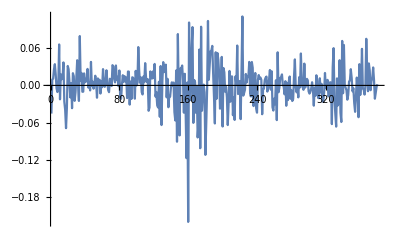

```mathematica
ListLinePlot[rsWethUsdc90dFiltered4HourCandle, PlotRange->All]
```

```mathematica
edistWethUsdc90dFiltered4HourCandle = EstimatedDistribution[rsWethUsdc90dFiltered4HourCandle, StableDistribution[1, aWU90dC4h, bWU90dC4h, locWU90dC4h, scaleWU90dC4h]]
```

StableDistribution[1,1.56948,-0.158903,-0.000646165,0.0176279]

```mathematica
0.007900125269736371 * (4^(1/1.6))
```

0.0187898

```mathematica
0.012614644025489237 * (2^(1/1.6))
```

0.0194544

```mathematica
(* 1h -> 4h looks good as well for c_long = N^(1/alpha) * c_short *)
```

```mathematica
rsWethUsdc90dFiltered6HourCandle = Differences[Log[twapsWethUsdc90dFiltered6HourCandle]]
```

{-0.0518826,0.0265779,0.0330679,0.0447344,-0.0114995,-0.0048604,0.0526756,0.0086456,0.0104686,0.0485962,-0.0744088,-0.0597538,0.00709897,0.0139123,0.00235,-0.0131275,-0.0263514,0.0241596,-0.0170633,-0.006891,0.0519437,-0.0353748,0.0825161,0.0246683,-0.00537136,0.00433166,0.0163504,0.00558811,0.0261509,0.00117001,-0.00677123,0.036069,0.00801432,-0.00572794,0.0226063,-0.0229739,0.00703565,0.0144693,-0.0131185,0.00386094,0.0308001,0.00236509,0.0262034,0.00485433,-0.0151823,0.00741029,0.0177545,0.0234846,0.0412579,0.00395485,0.0633158,-0.0087769,0.028767,-0.0267461,-0.00118163,-0.00264724,-0.00429902,0.0315494,0.0094134,0.00529828,0.00291087,-0.00547732,-0.00958727,0.0131436,0.00164081,0.00780864,0.0080955,0.057691,0.0277094,0.0137178,-0.0380579,0.0268427,0.0104384,0.0432644,-0.005133,-0.0200733,-0.0251593,0.024328,0.0172654,0.0280453,0.0261108,-0.0200934,-0.0257652,-0.0363118,-0.0487288,-0.0344689,0.061141,0.00508798,0.0554984,-0.0158076,-0.00393392,-0.0377388,-0.033191,0.0177157,-0.00171464,-0.0369136,-0.0740495,-0.0490687,0.0665531,-0.0819664,0.041094,0.0456567,-0.0376342,0.0206376,-0.0972823,-0.0542537,-0.0507174,-0.0916258,0.031503,0.106759,-0.0511022,0.00466147,-0.0197382,-0.109684,-0.021652,-0.0825147,0.0929268,-0.0560285,0.00464673,-0.126292,-0.0602533,0.0959468,0.00631673,0.0909115,0.0977173,0.0422165,-0.0160429,-0.0105019,0.0054115,0.0668831,0.0116294,-0.0383188,-0.00214632,0.00986977,0.026667,-0.0182526,-0.0362279,-0.0747263,0.00581313,0.00535353,-0.00621063,-0.0460798,-0.0567324,0.0161532,0.0527249,0.0012909,-0.0111261,-0.0120068,0.129685,-0.0473019,-0.00617979,0.0225264,0.035064,0.0320715,-0.0303331,0.0371457,0.00623919,-0.0100243,-0.0256427,-0.0353123,0.0107336,0.0251734,0.0186098,-0.0432667,-0.0121402,0.00851705,0.0159586,0.000813366,0.0045098,0.0260127,0.0173393,-0.0365687,-0.0506723,-0.0413056,-0.00367565,0.00939506,-0.0209492,0.0184832,0.0393639,-0.00747075,-0.0158685,0.00614828,-0.034994,-0.0174237,0.0150918,-0.0155163,-0.023231,-0.032027,0.0501457,0.00286587,-0.0138137,-0.0182636,0.00836038,0.0529739,0.00222649,-0.00562289,0.0422945,-0.00719802,0.0214195,-0.0124769,-0.00362773,-0.0248485,0.00937465,-0.0430563,-0.0106602,0.00692326,-0.00592808,-0.0280091,-0.00218022,0.00500865,-0.0434552,-0.0204299,-0.00713746,0.0186631,0.00373425,-0.0275413,0.0154446,-0.0684494,0.0532441,0.0157813,-0.0919158,-0.00870434,-0.0510033,0.0338979,-0.039737,0.00853656,0.0127828,0.0401885,-0.00828119,-0.0262796,-0.0187444,0.0176615,0.0421,-0.0130758,-0.0164787,-0.0590984,-0.000119747,-0.0159525,-0.0294693,-0.00300868,0.0338084,0.0233172,-0.0164223,-0.00554093,0.0774736,0.0134194,0.0465348,0.00502574,0.0242491,0.0239492,0.00480935,-0.0298776,-0.01519}

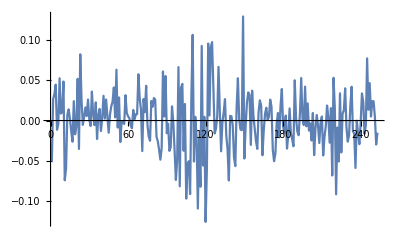

```mathematica
ListLinePlot[rsWethUsdc90dFiltered6HourCandle, PlotRange->All]
```

```mathematica
edistWethUsdc90dFiltered6HourCandle = EstimatedDistribution[rsWethUsdc90dFiltered6HourCandle, StableDistribution[1, aWU90dC6h, bWU90dC6h, locWU90dC6h, scaleWU90dC6h]]
```

StableDistribution[1,1.73971,-0.0744163,-0.000470773,0.0227901]

```mathematica
(* Not a good alpha here for 6h candle ... (not enough data?) *)
```

```mathematica
0.007900125269736371 / (6^(1/1.6))
```

0.00257804

```mathematica
edistWethUsdc90dFiltered
```

StableDistribution[1,1.46465,-0.0496207,-0.000010553,0.00154277]

```mathematica
edistWethUsdc90dFiltered30MinCandle
```

StableDistribution[1,1.55263,-0.0735773,-0.0000556332,0.00439438]

```mathematica
edistWethUsdc90dFiltered1HourCandle
```

StableDistribution[1,1.59768,-0.0971292,-0.000157254,0.00790013]

```mathematica
edistWethUsdc90dFiltered2HourCandle
```

StableDistribution[1,1.66239,-0.0643151,-0.000079592,0.0126146]

```mathematica
edistWethUsdc90dFiltered4HourCandle
```

StableDistribution[1,1.56948,-0.158903,-0.000646165,0.0176279]

```mathematica
edistWethUsdc90dFiltered6HourCandle
```

StableDistribution[1,1.73971,-0.0744163,-0.000470773,0.0227901]

```mathematica
(* Beta should linearly add up like loc as increase candle size if not consistent with zero. Unclear, but not behaving according to linear combo props of stable dist as nicely as scale is: so maybe zero? Enable fitting in pystable that fixes params? *)
```

```mathematica
0.007900125269736371 / (2^(1/1.6))
```

0.0051226

```mathematica
(* Actually the scale down from 1h -> 30m isn't terrible as well. *)
```

```mathematica
(* Seems a good place to estimate k values would be 1h candles ... see note-4.nb for k analysis there *)
```